## Correct dt = pi/8

### data

```mathematica
Ers={-0.000000000000000000*10^+00,1.999999999999999778*10^+00,3.999999999999998668*10^+00,3.999999999999998668*10^+00,3.999999999999998668*10^+00,1.999999999999999556*10^+00,1.999999999999999556*10^+00,1.999999999999999334*10^+00,9.610279511444749964*10^-16,1.999999999999999556*10^+00,3.999999999999996447*10^+00,3.999999999999996447*10^+00,1.999999999999999112*10^+00,6.406853007629834296*10^-16,6.406853007629834296*10^-16,6.406853007629834296*10^-16,6.406853007629834296*10^-16,1.999999999999999556*10^+00,3.999999999999997335*10^+00,3.999999999999997335*10^+00,3.999999999999996447*10^+00,1.999999999999999112*10^+00,1.999999999999999112*10^+00,1.999999999999998890*10^+00,1.999999999999998890*10^+00,3.999999999999994671*10^+00,1.999999999999998668*10^+00,1.999999999999998668*10^+00,3.999999999999992006*10^+00,1.999999999999998224*10^+00,1.999999999999998224*10^+00,1.999999999999998002*10^+00,6.727195658011310973*10^-15,1.999999999999997780*10^+00,3.999999999999986677*10^+00,3.999999999999986677*10^+00,3.999999999999986677*10^+00,1.999999999999996669*10^+00,1.999999999999996669*10^+00,1.999999999999996669*10^+00,6.406853007629821477*10^-15,1.999999999999997335*10^+00,3.999999999999988010*10^+00,3.999999999999988010*10^+00,1.999999999999997113*10^+00,5.445825056485349833*10^-15,5.445825056485349833*10^-15,5.445825056485349833*10^-15,1.999999999999998002*10^+00,3.999999999999989342*10^+00,1.999999999999997335*10^+00,1.999999999999997113*10^+00,1.999999999999997113*10^+00,9.289936861063230886*10^-15,9.930622161826211456*10^-15,9.930622161826211456*10^-15,1.057130746258919045*10^-14,1.999999999999996003*10^+00,3.999999999999980460*10^+00,3.999999999999980460*10^+00,1.999999999999995559*10^+00,1.569678986869301292*10^-14,1.633747516945598718*10^-14,1.633747516945598718*10^-14,1.697816047021896459*10^-14,1.999999999999993561*10^+00,3.999999999999968914*10^+00,3.999999999999968914*10^+00,3.999999999999968470*10^+00,1.999999999999993117*10^+00,1.999999999999993117*10^+00,1.999999999999992895*10^+00,1.890021637250789053*10^-14,1.999999999999992673*10^+00,3.999999999999965361*10^+00,3.999999999999965361*10^+00,1.999999999999992006*10^+00,2.018158697403384220*10^-14,2.018158697403384220*10^-14,2.018158697403384220*10^-14,2.018158697403384220*10^-14,1.999999999999992006*10^+00,3.999999999999962697*10^+00,3.999999999999962697*10^+00,3.999999999999961808*10^+00,1.999999999999991562*10^+00,1.999999999999991562*10^+00,1.999999999999991562*10^+00,1.999999999999991562*10^+00,3.999999999999959144*10^+00,1.999999999999991118*10^+00,1.999999999999990674*10^+00,3.999999999999957812*10^+00,1.999999999999990674*10^+00,1.999999999999990674*10^+00,1.999999999999990452*10^+00,1.999999999999990452*10^+00,3.999999999999955591*10^+00,1.999999999999989786*10^+00,1.999999999999989786*10^+00,1.999999999999989786*10^+00,2.562741203051911551*10^-14,2.562741203051911551*10^-14,2.562741203051911551*10^-14,1.999999999999990008*10^+00,3.999999999999953371*10^+00,1.999999999999989342*10^+00,1.999999999999989342*10^+00,3.999999999999949818*10^+00,1.999999999999988898*10^+00,1.999999999999988898*10^+00,1.999999999999988676*10^+00,2.722912528242654327*10^-14,1.999999999999989342*10^+00,3.999999999999950262*10^+00,3.999999999999950262*10^+00,3.999999999999950262*10^+00,1.999999999999988898*10^+00,1.999999999999988898*10^+00,1.999999999999988898*10^+00,1.999999999999988898*10^+00,3.999999999999948042*10^+00,1.999999999999988676*10^+00,1.999999999999988232*10^+00,3.999999999999944933*10^+00,1.999999999999987566*10^+00,1.999999999999987566*10^+00,1.999999999999988010*10^+00,3.491734889158217758*10^-14,1.999999999999986455*10^+00,3.999999999999937383*10^+00,3.999999999999937383*10^+00,3.999999999999936939*10^+00,1.999999999999986011*10^+00,1.999999999999986011*10^+00,1.999999999999986011*10^+00,3.683940479387108458*10^-14,1.999999999999985345*10^+00,3.999999999999932943*10^+00,3.999999999999932943*10^+00,1.999999999999985345*10^+00,3.876146069615998527*10^-14,3.876146069615998527*10^-14,3.876146069615998527*10^-14,3.876146069615998527*10^-14,1.999999999999984901*10^+00,3.999999999999931166*10^+00,3.999999999999931166*10^+00,3.999999999999930278*10^+00,1.999999999999984457*10^+00,1.999999999999984457*10^+00,1.999999999999984457*10^+00,1.999999999999984457*10^+00,3.999999999999926725*10^+00,1.999999999999983791*10^+00,1.999999999999983569*10^+00,3.999999999999924505*10^+00,1.999999999999983347*10^+00,1.999999999999983347*10^+00,1.999999999999983125*10^+00,4.516831370378963320*10^-14,1.999999999999982236*10^+00,3.999999999999920064*10^+00,3.999999999999920064*10^+00,3.999999999999919176*10^+00,1.999999999999982236*10^+00,1.999999999999982236*10^+00,1.999999999999982236*10^+00,4.452762840302666840*10^-14,1.999999999999982458*10^+00,3.999999999999919176*10^+00,3.999999999999919176*10^+00,1.999999999999982458*10^+00,4.420728575264518285*10^-14,4.420728575264518285*10^-14,4.420728575264518285*10^-14,1.999999999999982903*10^+00,3.999999999999920064*10^+00,1.999999999999982236*10^+00,1.999999999999982458*10^+00,1.999999999999982236*10^+00,4.548865635417111875*10^-14,4.612934165493407723*10^-14,4.612934165493407723*10^-14,4.677002695569704202*10^-14,1.999999999999982014*10^+00,3.999999999999915179*10^+00,3.999999999999915179*10^+00,1.999999999999981348*10^+00,4.837174020760444454*10^-14,4.901242550836740933*10^-14,4.901242550836740933*10^-14,1.999999999999981126*10^+00,3.999999999999912959*10^+00,1.999999999999981126*10^+00,1.999999999999980682*10^+00,1.999999999999980682*10^+00,4.677002695569704202*10^-14,4.677002695569704202*10^-14,4.677002695569704202*10^-14,2.722912528242654327*10^-14,1.999999999999909406*10^+00,3.999999999999998668*10^+00,3.999999999999998668*10^+00,3.999999999999998668*10^+00,2.271698979605548452*10^+00,2.271698979605548452*10^+00,2.271698979605547564*10^+00,3.222555369723181795*10^-01,2.272682602232312110*10^+00,3.861653111783584613*10^+00,3.861653111783583725*10^+00,2.272682602232312554*10^+00,3.222555369723191232*10^-01,3.222555369723190677*10^-01,3.222555369723190677*10^-01,3.222555369723193452*10^-01,2.272682602232312110*10^+00,3.861653111783585057*10^+00,3.861653111783584613*10^+00,3.861653111783583725*10^+00,1.929680324037555739*10^+00,1.929680324037556183*10^+00,1.929680324037555739*10^+00,1.929680324037555739*10^+00,3.861653111783581505*10^+00,2.272682602232310334*10^+00,2.272682602232310334*10^+00,3.861653111783578840*10^+00,1.929680324037554850*10^+00,1.929680324037554850*10^+00,1.929680324037554850*10^+00,3.507752021677292351*10^-14,1.999999999999906297*10^+00,3.999999999999985789*10^+00,3.999999999999985789*10^+00,3.999999999999985789*10^+00,2.271698979605543567*10^+00,2.271698979605543567*10^+00,2.271698979605543123*10^+00,3.222555369723246743*10^-01,2.272682602232306781*10^+00,3.861653111783570402*10^+00,3.861653111783569958*10^+00,2.272682602232306337*10^+00,3.222555369723253960*10^-01,3.222555369723247298*10^-01,3.222555369723247298*10^-01,2.271698979605542679*10^+00,3.999999999999983125*10^+00,1.999999999999905853*10^+00,1.999999999999905631*10^+00,1.999999999999905187*10^+00,3.940214599692294375*10^-14,4.004283129768591486*10^-14,4.004283129768591486*10^-14,4.068351659844887965*10^-14,1.999999999999904077*10^+00,3.999999999999974687*10^+00,3.999999999999974687*10^+00,1.999999999999903633*10^+00,4.292591515111925958*10^-14,4.356660045188222437*10^-14,4.356660045188222437*10^-14,4.420728575264518285*10^-14,1.999999999999902744*10^+00,3.999999999999968914*10^+00,3.999999999999968914*10^+00,3.999999999999968026*10^+00,2.271698979605537350*10^+00,2.271698979605537350*10^+00,2.271698979605537794*10^+00,3.222555369723333341*10^-01,2.272682602232301008*10^+00,3.861653111783553971*10^+00,3.861653111783554415*10^+00,2.272682602232301452*10^+00,3.222555369723332230*10^-01,3.222555369723331120*10^-01,3.222555369723331120*10^-01,3.222555369723327789*10^-01,2.272682602232300564*10^+00,3.861653111783550862*10^+00,3.861653111783551751*10^+00,3.861653111783550862*10^+00,1.929680324037549521*10^+00,1.929680324037549299*10^+00,1.929680324037549743*10^+00,1.929680324037549299*10^+00,3.861653111783548642*10^+00,2.272682602232299232*10^+00,2.272682602232298787*10^+00,3.861653111783546422*10^+00,1.929680324037548189*10^+00,1.929680324037548411*10^+00,1.929680324037548411*10^+00,1.929680324037548411*10^+00,3.861653111783543313*10^+00,2.272682602232297455*10^+00,2.272682602232297455*10^+00,2.272682602232297455*10^+00,3.222555369723368313*10^-01,3.222555369723367202*10^-01,3.222555369723367202*10^-01,2.271698979605533797*10^+00,3.999999999999955147*10^+00,1.999999999999899192*10^+00,1.999999999999899192*10^+00,3.999999999999952927*10^+00,2.271698979605532021*10^+00,2.271698979605532021*10^+00,2.271698979605532021*10^+00,3.222555369723377749*10^-01,2.272682602232296123*10^+00,3.861653111783540204*10^+00,3.861653111783541092*10^+00,3.861653111783539316*10^+00,1.929680324037547079*10^+00,1.929680324037547079*10^+00,1.929680324037547301*10^+00,1.929680324037547079*10^+00,3.861653111783537096*10^+00,2.272682602232293902*10^+00,2.272682602232294347*10^+00,3.861653111783534431*10^+00,1.929680324037546191*10^+00,1.929680324037545747*10^+00,1.929680324037545747*10^+00,6.070493224729141425*10^-14,1.999999999999896527*10^+00,3.999999999999940048*10^+00,3.999999999999940048*10^+00,3.999999999999939604*10^+00,2.271698979605528912*10^+00,2.271698979605528912*10^+00,2.271698979605527580*10^+00,3.222555369723443808*10^-01,2.272682602232292126*10^+00,3.861653111783528658*10^+00,3.861653111783528214*10^+00,2.272682602232291682*10^+00,3.222555369723455465*10^-01,3.222555369723462126*10^-01,3.222555369723462126*10^-01,3.222555369723457686*10^-01,2.272682602232290794*10^+00,3.861653111783525549*10^+00,3.861653111783525993*10^+00,3.861653111783525105*10^+00,1.929680324037543970*10^+00,1.929680324037543970*10^+00,1.929680324037543970*10^+00,1.929680324037543748*10^+00,3.861653111783522885*10^+00,2.272682602232288573*10^+00,2.272682602232289018*10^+00,3.861653111783520664*10^+00,1.929680324037542860*10^+00,1.929680324037543082*10^+00,1.929680324037542638*10^+00,6.919401248240056364*10^-14,1.999999999999893197*10^+00,3.999999999999924949*10^+00,3.999999999999924949*10^+00,3.999999999999924505*10^+00,2.271698979605523139*10^+00,2.271698979605523139*10^+00,2.271698979605523139*10^+00,3.222555369723513197*10^-01,2.272682602232286797*10^+00,3.861653111783511783*10^+00,3.861653111783511783*10^+00,2.272682602232286797*10^+00,3.222555369723522078*10^-01,3.222555369723522078*10^-01,3.222555369723522078*10^-01,2.271698979605522251*10^+00,3.999999999999921840*10^+00,1.999999999999892086*10^+00,1.999999999999892086*10^+00,1.999999999999891864*10^+00,7.463983753888564763*10^-14,7.528052283964860611*10^-14,7.528052283964860611*10^-14,7.592120814041155197*10^-14,1.999999999999890310*10^+00,3.999999999999912959*10^+00,3.999999999999912959*10^+00,1.999999999999890310*10^+00,7.848394934346334803*10^-14,7.896446331903556690*10^-14,7.896446331903556690*10^-14,1.929680324037538863*10^+00,3.861653111783498016*10^+00,2.272682602232281912*10^+00,2.272682602232280580*10^+00,2.272682602232280580*10^+00,3.222555369723586471*10^-01,3.222555369723594243*10^-01,3.222555369723594243*10^-01,-9.610279511444755881*10^-16,2.000000000000000000*10^+00,4.000000000000000000*10^+00,4.000000000000000000*10^+00,4.000000000000000000*10^+00,2.656573126263760187*10^+00,2.656573126263760187*10^+00,2.656573126263759743*10^+00,8.791474266370062907*10^-01,2.688023245319977494*10^+00,3.492420773830301695*10^+00,3.492420773830301250*10^+00,2.688023245319977050*10^+00,8.791474266370060686*10^-01,8.791474266370059576*10^-01,8.791474266370059576*10^-01,8.791474266370057356*10^-01,2.688023245319975718*10^+00,3.492420773830300806*10^+00,3.492420773830301695*10^+00,3.492420773830300806*10^+00,1.729030204872845422*10^+00,1.729030204872845644*10^+00,1.729030204872845422*10^+00,1.729030204872845200*10^+00,3.492420773830298586*10^+00,2.688023245319974386*10^+00,2.688023245319973942*10^+00,3.492420773830297698*10^+00,1.729030204872844756*10^+00,1.729030204872844756*10^+00,1.729030204872844978*10^+00,7.207709633583546400*10^-15,1.999999999999997558*10^+00,3.999999999999988010*10^+00,3.999999999999988010*10^+00,3.999999999999986677*10^+00,2.656573126263753526*10^+00,2.656573126263753526*10^+00,2.656573126263752638*10^+00,8.791474266370088442*10^-01,2.688023245319969945*10^+00,3.492420773830290592*10^+00,3.492420773830291481*10^+00,2.688023245319969501*10^+00,8.791474266370089552*10^-01,8.791474266370087332*10^-01,8.791474266370087332*10^-01,2.656573126263751750*10^+00,3.999999999999985345*10^+00,1.999999999999996447*10^+00,1.999999999999996225*10^+00,1.999999999999996447*10^+00,1.185267806411514685*10^-14,1.249336336487812427*10^-14,1.249336336487812427*10^-14,1.329421999083184604*10^-14,1.999999999999995115*10^+00,3.999999999999976463*10^+00,3.999999999999976463*10^+00,1.999999999999994671*10^+00,1.601713251907450163*10^-14,1.665781781983747589*10^-14,1.665781781983747589*10^-14,1.729850312060045014*10^-14,1.999999999999993561*10^+00,3.999999999999968914*10^+00,3.999999999999968914*10^+00,3.999999999999968470*10^+00,2.656573126263745088*10^+00,2.656573126263745088*10^+00,2.656573126263744644*10^+00,8.791474266370142843*10^-01,2.688023245319961063*10^+00,3.492420773830276381*10^+00,3.492420773830275937*10^+00,2.688023245319960619*10^+00,8.791474266370129520*10^-01,8.791474266370129520*10^-01,8.791474266370129520*10^-01,8.791474266370137292*10^-01,2.688023245319960175*10^+00,3.492420773830274605*10^+00,3.492420773830275049*10^+00,3.492420773830274161*10^+00,1.729030204872842091*10^+00,1.729030204872842091*10^+00,1.729030204872841869*10^+00,1.729030204872841425*10^+00,3.492420773830273273*10^+00,2.688023245319957955*10^+00,2.688023245319957955*10^+00,3.492420773830271052*10^+00,1.729030204872840981*10^+00,1.729030204872840981*10^+00,1.729030204872841203*10^+00,1.729030204872841203*10^+00,3.492420773830268388*10^+00,2.688023245319955290*10^+00,2.688023245319954846*10^+00,2.688023245319955734*10^+00,8.791474266370157276*10^-01,8.791474266370153945*10^-01,8.791474266370153945*10^-01,2.656573126263738871*10^+00,3.999999999999956035*10^+00,1.999999999999990230*10^+00,1.999999999999990008*10^+00,3.999999999999953815*10^+00,2.656573126263737095*10^+00,2.656573126263737095*10^+00,2.656573126263736651*10^+00,8.791474266370160606*10^-01,2.688023245319953070*10^+00,3.492420773830266612*10^+00,3.492420773830266167*10^+00,3.492420773830264391*10^+00,1.729030204872840315*10^+00,1.729030204872840759*10^+00,1.729030204872840315*10^+00,1.729030204872840759*10^+00,3.492420773830263059*10^+00,2.688023245319950405*10^+00,2.688023245319950405*10^+00,3.492420773830260838*10^+00,1.729030204872839649*10^+00,1.729030204872839871*10^+00,1.729030204872839649*10^+00,3.267495033891179134*10^-14,1.999999999999987566*10^+00,3.999999999999941380*10^+00,3.999999999999941380*10^+00,3.999999999999940492*10^+00,2.656573126263730877*10^+00,2.656573126263730877*10^+00,2.656573126263730433*10^+00,8.791474266370192803*10^-01,2.688023245319945964*10^+00,3.492420773830255509*10^+00,3.492420773830254621*10^+00,2.688023245319945964*10^+00,8.791474266370192803*10^-01,8.791474266370193913*10^-01,8.791474266370193913*10^-01,8.791474266370198354*10^-01,2.688023245319946852*10^+00,3.492420773830255065*10^+00,3.492420773830254621*10^+00,3.492420773830253733*10^+00,1.729030204872838761*10^+00,1.729030204872839205*10^+00,1.729030204872838761*10^+00,1.729030204872838539*10^+00,3.492420773830252401*10^+00,2.688023245319944188*10^+00,2.688023245319944188*10^+00,3.492420773830249736*10^+00,1.729030204872838317*10^+00,1.729030204872838317*10^+00,1.729030204872838317*10^+00,4.148437322440259037*10^-14,1.999999999999984013*10^+00,3.999999999999926725*10^+00,3.999999999999926725*10^+00,3.999999999999926281*10^+00,2.656573126263723328*10^+00,2.656573126263723328*10^+00,2.656573126263724660*10^+00,8.791474266370229440*10^-01,2.688023245319940191*10^+00,3.492420773830243963*10^+00,3.492420773830243963*10^+00,2.688023245319939303*10^+00,8.791474266370226109*10^-01,8.791474266370226109*10^-01,8.791474266370226109*10^-01,2.656573126263723772*10^+00,3.999999999999924061*10^+00,1.999999999999983125*10^+00,1.999999999999982903*10^+00,1.999999999999982903*10^+00,4.644968430531555647*10^-14,4.725054093126926089*10^-14,4.741071225646000051*10^-14,4.805139755722296530*10^-14,1.999999999999981792*10^+00,3.999999999999914735*10^+00,3.999999999999914735*10^+00,1.999999999999981126*10^+00,5.093448141065629109*10^-14,5.157516671141925588*10^-14,5.157516671141925588*10^-14,1.729030204872835430*10^+00,3.492420773830230640*10^+00,2.688023245319931309*10^+00,2.688023245319931753*10^+00,2.688023245319931753*10^+00,8.791474266370269408*10^-01,8.791474266370270518*10^-01,8.791474266370270518*10^-01,9.610279511444749964*10^-16,1.999999999999999778*10^+00,3.999999999999998224*10^+00,3.999999999999998224*10^+00,3.999999999999997335*10^+00,2.868623331691849465*10^+00,2.868623331691849465*10^+00,2.868623331691849021*10^+00,1.381219592801851581*10^+00,3.080517531469032733*10^+00,3.010703857714096543*10^+00,3.010703857714096543*10^+00,3.080517531469032733*10^+00,1.381219592801850915*10^+00,1.381219592801851137*10^+00,1.381219592801850915*10^+00,1.381219592801850471*10^+00,3.080517531469032733*10^+00,3.010703857714097431*10^+00,3.010703857714097875*10^+00,3.010703857714096099*10^+00,1.427593131110275415*10^+00,1.427593131110275859*10^+00,1.427593131110275637*10^+00,1.427593131110275859*10^+00,3.010703857714096099*10^+00,3.080517531469030068*10^+00,3.080517531469030512*10^+00,3.010703857714093878*10^+00,1.427593131110275193*10^+00,1.427593131110275415*10^+00,1.427593131110274971*10^+00,7.367880958774292331*10^-15,1.999999999999997335*10^+00,3.999999999999986233*10^+00,3.999999999999986233*10^+00,3.999999999999984901*10^+00,2.868623331691843248*10^+00,2.868623331691843248*10^+00,2.868623331691842360*10^+00,1.381219592801851581*10^+00,3.080517531469024295*10^+00,3.010703857714089438*10^+00,3.010703857714089438*10^+00,3.080517531469023407*10^+00,1.381219592801851359*10^+00,1.381219592801851803*10^+00,1.381219592801851803*10^+00,2.868623331691840583*10^+00,3.999999999999980904*10^+00,1.999999999999995559*10^+00,1.999999999999995337*10^+00,1.999999999999995559*10^+00,1.345439131602259039*10^-14,1.425524794197631216*10^-14,1.425524794197631216*10^-14,1.489593324273928957*10^-14,1.999999999999994671*10^+00,3.999999999999972911*10^+00,3.999999999999972911*10^+00,1.999999999999994005*10^+00,1.729850312060045014*10^-14,1.793918842136342756*10^-14,1.793918842136342756*10^-14,1.857987372212640182*10^-14,1.999999999999992895*10^+00,3.999999999999966693*10^+00,3.999999999999966693*10^+00,3.999999999999965361*10^+00,2.868623331691831702*10^+00,2.868623331691831702*10^+00,2.868623331691832146*10^+00,1.381219592801853135*10^+00,3.080517531469011860*10^+00,3.010703857714076559*10^+00,3.010703857714076559*10^+00,3.080517531469010528*10^+00,1.381219592801852025*10^+00,1.381219592801852247*10^+00,1.381219592801852247*10^+00,1.381219592801852025*10^+00,3.080517531469010972*10^+00,3.010703857714076115*10^+00,3.010703857714076559*10^+00,3.010703857714075671*10^+00,1.427593131110275859*10^+00,1.427593131110275859*10^+00,1.427593131110275415*10^+00,1.427593131110275415*10^+00,3.010703857714074339*10^+00,3.080517531469007420*10^+00,3.080517531469008752*10^+00,3.010703857714073450*10^+00,1.427593131110275193*10^+00,1.427593131110275415*10^+00,1.427593131110275193*10^+00,1.427593131110275415*10^+00,3.010703857714071674*10^+00,3.080517531469006087*10^+00,3.080517531469004311*10^+00,3.080517531469004311*10^+00,1.381219592801852247*10^+00,1.381219592801852247*10^+00,1.381219592801852247*10^+00,2.868623331691825484*10^+00,3.999999999999953815*10^+00,1.999999999999989564*10^+00,1.999999999999989564*10^+00,3.999999999999951150*10^+00,2.868623331691823264*10^+00,2.868623331691823264*10^+00,2.868623331691822376*10^+00,1.381219592801851581*10^+00,3.080517531469002535*10^+00,3.010703857714070342*10^+00,3.010703857714070342*10^+00,3.010703857714069898*10^+00,1.427593131110276303*10^+00,1.427593131110276303*10^+00,1.427593131110276303*10^+00,1.427593131110276303*10^+00,3.010703857714067677*10^+00,3.080517531468999870*10^+00,3.080517531468999870*10^+00,3.010703857714066345*10^+00,1.427593131110275859*10^+00,1.427593131110276303*10^+00,1.427593131110275415*10^+00,3.267495033891179134*10^-14,1.999999999999987566*10^+00,3.999999999999940936*10^+00,3.999999999999940936*10^+00,3.999999999999940492*10^+00,2.868623331691817491*10^+00,2.868623331691817491*10^+00,2.868623331691816603*10^+00,1.381219592801852247*10^+00,3.080517531468994541*10^+00,3.010703857714060572*10^+00,3.010703857714061016*10^+00,3.080517531468993209*10^+00,1.381219592801851803*10^+00,1.381219592801852247*10^+00,1.381219592801852247*10^+00,1.381219592801852025*10^+00,3.080517531468993209*10^+00,3.010703857714062348*10^+00,3.010703857714062348*10^+00,3.010703857714061904*10^+00,1.427593131110276747*10^+00,1.427593131110276969*10^+00,1.427593131110276303*10^+00,1.427593131110276747*10^+00,3.010703857714061016*10^+00,3.080517531468990988*10^+00,3.080517531468990988*10^+00,3.010703857714059684*10^+00,1.427593131110276303*10^+00,1.427593131110276303*10^+00,1.427593131110275859*10^+00,3.924197467173221044*10^-14,1.999999999999984901*10^+00,3.999999999999929834*10^+00,3.999999999999929834*10^+00,3.999999999999929390*10^+00,2.868623331691810385*10^+00,2.868623331691810385*10^+00,2.868623331691809941*10^+00,1.381219592801852025*10^+00,3.080517531468986991*10^+00,3.010703857714056575*10^+00,3.010703857714056131*10^+00,3.080517531468986103*10^+00,1.381219592801851803*10^+00,1.381219592801851803*10^+00,1.381219592801851803*10^+00,2.868623331691808609*10^+00,3.999999999999925393*10^+00,1.999999999999983569*10^+00,1.999999999999983347*10^+00,1.999999999999983347*10^+00,4.404711442745444323*10^-14,4.452762840302666840*10^-14,4.452762840302666840*10^-14,4.516831370378963320*10^-14,1.999999999999982681*10^+00,3.999999999999919176*10^+00,3.999999999999919176*10^+00,1.999999999999982236*10^+00,4.805139755722296530*10^-14,4.853191153279518416*10^-14,4.853191153279518416*10^-14,1.427593131110276303*10^+00,3.010703857714048137*10^+00,3.080517531468977666*10^+00,3.080517531468977666*10^+00,3.080517531468977666*10^+00,1.381219592801853135*10^+00,1.381219592801852691*10^+00,1.381219592801852691*10^+00,4.805139755722374982*10^-16,1.999999999999999556*10^+00,3.999999999999997335*10^+00,3.999999999999997335*10^+00,3.999999999999997335*10^+00,2.854405313558543877*10^+00,2.854405313558543877*10^+00,2.854405313558542989*10^+00,1.726492313244599508*10^+00,3.380661745880490177*10^+00,2.532435416257526661*10^+00,2.532435416257526661*10^+00,3.380661745880489732*10^+00,1.726492313244598620*10^+00,1.726492313244598176*10^+00,1.726492313244598176*10^+00,1.726492313244598620*10^+00,3.380661745880488400*10^+00,2.532435416257525773*10^+00,2.532435416257526217*10^+00,2.532435416257525773*10^+00,1.070009614893125072*10^+00,1.070009614893125294*10^+00,1.070009614893124628*10^+00,1.070009614893125072*10^+00,2.532435416257524885*10^+00,3.380661745880485292*10^+00,3.380661745880485736*10^+00,2.532435416257523553*10^+00,1.070009614893125072*10^+00,1.070009614893125516*10^+00,1.070009614893125516*10^+00,9.930622161826211456*10^-15,1.999999999999996003*10^+00,3.999999999999980460*10^+00,3.999999999999980460*10^+00,3.999999999999979572*10^+00,2.854405313558536328*10^+00,2.854405313558536328*10^+00,2.854405313558535440*10^+00,1.726492313244597288*10^+00,3.380661745880478186*10^+00,2.532435416257520888*10^+00,2.532435416257520000*10^+00,3.380661745880478186*10^+00,1.726492313244596399*10^+00,1.726492313244596399*10^+00,1.726492313244596399*10^+00,2.854405313558534107*10^+00,3.999999999999975131*10^+00,1.999999999999994227*10^+00,1.999999999999994005*10^+00,1.999999999999994227*10^+00,1.601713251907450163*10^-14,1.665781781983747589*10^-14,1.665781781983747589*10^-14,1.713833179540970737*10^-14,1.999999999999993339*10^+00,3.999999999999968470*10^+00,3.999999999999968470*10^+00,1.999999999999992895*10^+00,1.954090167327086478*10^-14,2.002141564884309627*10^-14,1.986124432365235034*10^-14,2.066210094960607053*10^-14,1.999999999999992006*10^+00,3.999999999999961808*10^+00,3.999999999999961808*10^+00,3.999999999999961364*10^+00,2.854405313558525670*10^+00,2.854405313558525670*10^+00,2.854405313558525670*10^+00,1.726492313244594623*10^+00,3.380661745880463975*10^+00,2.532435416257514227*10^+00,2.532435416257513339*10^+00,3.380661745880463531*10^+00,1.726492313244593957*10^+00,1.726492313244593957*10^+00,1.726492313244593957*10^+00,1.726492313244593735*10^+00,3.380661745880463087*10^+00,2.532435416257513339*10^+00,2.532435416257513339*10^+00,2.532435416257513783*10^+00,1.070009614893132843*10^+00,1.070009614893132621*10^+00,1.070009614893132399*10^+00,1.070009614893132399*10^+00,2.532435416257512895*10^+00,3.380661745880460423*10^+00,3.380661745880459534*10^+00,2.532435416257511562*10^+00,1.070009614893132621*10^+00,1.070009614893132177*10^+00,1.070009614893132621*10^+00,1.070009614893132621*10^+00,2.532435416257511118*10^+00,3.380661745880457758*10^+00,3.380661745880455982*10^+00,3.380661745880455982*10^+00,1.726492313244592847*10^+00,1.726492313244592625*10^+00,1.726492313244592625*10^+00,2.854405313558518564*10^+00,3.999999999999945821*10^+00,1.999999999999988010*10^+00,1.999999999999987788*10^+00,3.999999999999943601*10^+00,2.854405313558514568*10^+00,2.854405313558514568*10^+00,2.854405313558516788*10^+00,1.726492313244591070*10^+00,3.380661745880449764*10^+00,2.532435416257508454*10^+00,2.532435416257508454*10^+00,2.532435416257508898*10^+00,1.070009614893135508*10^+00,1.070009614893135508*10^+00,1.070009614893135286*10^+00,1.070009614893135286*10^+00,2.532435416257506677*10^+00,3.380661745880447544*10^+00,3.380661745880447100*10^+00,2.532435416257506233*10^+00,1.070009614893135730*10^+00,1.070009614893135730*10^+00,1.070009614893136174*10^+00,3.796060407020627455*10^-14,1.999999999999985345*10^+00,3.999999999999931166*10^+00,3.999999999999931166*10^+00,3.999999999999930722*10^+00,2.854405313558508794*10^+00,2.854405313558508794*10^+00,2.854405313558508794*10^+00,1.726492313244590404*10^+00,3.380661745880439550*10^+00,2.532435416257500904*10^+00,2.532435416257501348*10^+00,3.380661745880437330*10^+00,1.726492313244590182*10^+00,1.726492313244590182*10^+00,1.726492313244590182*10^+00,1.726492313244589738*10^+00,3.380661745880437774*10^+00,2.532435416257501348*10^+00,2.532435416257501348*10^+00,2.532435416257500460*10^+00,1.070009614893138616*10^+00,1.070009614893138838*10^+00,1.070009614893138394*10^+00,1.070009614893138838*10^+00,2.532435416257499572*10^+00,3.380661745880433333*10^+00,3.380661745880434221*10^+00,2.532435416257498240*10^+00,1.070009614893139060*10^+00,1.070009614893138838*10^+00,1.070009614893139060*10^+00,4.773105490684148606*10^-14,1.999999999999981348*10^+00,3.999999999999913847*10^+00,3.999999999999913847*10^+00,3.999999999999912959*10^+00,2.854405313558500801*10^+00,2.854405313558500801*10^+00,2.854405313558500357*10^+00,1.726492313244588406*10^+00,3.380661745880425784*10^+00,2.532435416257494243*10^+00,2.532435416257495131*10^+00,3.380661745880424895*10^+00,1.726492313244587962*10^+00,1.726492313244587962*10^+00,1.726492313244587962*10^+00,2.854405313558499024*10^+00,3.999999999999908962*10^+00,1.999999999999980016*10^+00,1.999999999999979572*10^+00,1.999999999999979794*10^+00,5.349722261370813764*10^-14,5.413790791447108981*10^-14,5.397773658928035019*10^-14,5.445825056485256905*10^-14,1.999999999999978684*10^+00,3.999999999999902744*10^+00,3.999999999999902744*10^+00,1.999999999999978462*10^+00,5.702099176790440298*10^-14,5.750150574347662184*10^-14,5.750150574347662184*10^-14,1.070009614893142169*10^+00,2.532435416257488914*10^+00,3.380661745880416014*10^+00,3.380661745880416014*10^+00,3.380661745880416014*10^+00,1.726492313244586629*10^+00,1.726492313244586629*10^+00,1.726492313244586629*10^+00,3.203426503814917641*10^-16,2.000000000000000000*10^+00,3.999999999999998668*10^+00,3.999999999999998668*10^+00,3.999999999999997780*10^+00,2.618675334323285142*10^+00,2.618675334323285142*10^+00,2.618675334323285586*10^+00,1.908868005849928995*10^+00,3.635133706112523733*10^+00,2.231720244323815106*10^+00,2.231720244323814217*10^+00,3.635133706112522400*10^+00,1.908868005849928551*10^+00,1.908868005849928551*10^+00,1.908868005849928551*10^+00,1.908868005849928551*10^+00,3.635133706112520180*10^+00,2.231720244323814217*10^+00,2.231720244323814661*10^+00,2.231720244323814661*10^+00,7.091578053305445106*10^-01,7.091578053305441776*10^-01,7.091578053305445106*10^-01,7.091578053305442886*10^-01,2.231720244323813329*10^+00,3.635133706112518404*10^+00,3.635133706112517515*10^+00,2.231720244323812885*10^+00,7.091578053305452878*10^-01,7.091578053305456208*10^-01,7.091578053305457319*10^-01,1.009079348701695423*10^-14,1.999999999999996225*10^+00,3.999999999999981348*10^+00,3.999999999999981348*10^+00,3.999999999999980460*10^+00,2.618675334323278481*10^+00,2.618675334323278481*10^+00,2.618675334323278925*10^+00,1.908868005849925664*10^+00,3.635133706112508190*10^+00,2.231720244323810221*10^+00,2.231720244323810221*10^+00,3.635133706112507745*10^+00,1.908868005849924998*10^+00,1.908868005849924776*10^+00,1.908868005849924776*10^+00,2.618675334323278481*10^+00,3.999999999999973799*10^+00,1.999999999999994227*10^+00,1.999999999999994005*10^+00,1.999999999999994005*10^+00,1.649764649464672995*10^-14,1.697816047021896459*10^-14,1.697816047021896459*10^-14,1.761884577098193885*10^-14,1.999999999999993339*10^+00,3.999999999999968026*10^+00,3.999999999999968026*10^+00,1.999999999999992895*10^+00,1.938073034808011885*10^-14,2.002141564884309627*10^-14,2.002141564884309627*10^-14,2.050192962441532775*10^-14,1.999999999999992006*10^+00,3.999999999999963585*10^+00,3.999999999999963585*10^+00,3.999999999999962697*10^+00,2.618675334323271819*10^+00,2.618675334323271819*10^+00,2.618675334323270487*10^+00,1.908868005849922111*10^+00,3.635133706112492646*10^+00,2.231720244323804891*10^+00,2.231720244323805780*10^+00,3.635133706112491314*10^+00,1.908868005849921667*10^+00,1.908868005849921445*10^+00,1.908868005849921445*10^+00,1.908868005849921445*10^+00,3.635133706112489538*10^+00,2.231720244323804891*10^+00,2.231720244323805336*10^+00,2.231720244323805336*10^+00,7.091578053305563900*10^-01,7.091578053305562790*10^-01,7.091578053305567231*10^-01,7.091578053305565010*10^-01,2.231720244323803559*10^+00,3.635133706112487317*10^+00,3.635133706112485985*10^+00,2.231720244323803115*10^+00,7.091578053305576113*10^-01,7.091578053305573892*10^-01,7.091578053305580553*10^-01,7.091578053305576113*10^-01,2.231720244323802671*10^+00,3.635133706112482432*10^+00,3.635133706112483321*10^+00,3.635133706112483321*10^+00,1.908868005849919669*10^+00,1.908868005849919669*10^+00,1.908868005849919669*10^+00,2.618675334323265602*10^+00,3.999999999999944933*10^+00,1.999999999999987566*10^+00,1.999999999999987566*10^+00,3.999999999999942268*10^+00,2.618675334323263382*10^+00,2.618675334323263382*10^+00,2.618675334323263382*10^+00,1.908868005849918337*10^+00,3.635133706112475771*10^+00,2.231720244323800006*10^+00,2.231720244323800006*10^+00,2.231720244323800451*10^+00,7.091578053305616081*10^-01,7.091578053305617191*10^-01,7.091578053305618301*10^-01,7.091578053305619411*10^-01,2.231720244323798674*10^+00,3.635133706112472662*10^+00,3.635133706112472218*10^+00,2.231720244323799118*10^+00,7.091578053305631624*10^-01,7.091578053305622742*10^-01,7.091578053305632734*10^-01,3.892163202135072489*10^-14,1.999999999999984679*10^+00,3.999999999999929834*10^+00,3.999999999999929834*10^+00,3.999999999999929390*10^+00,2.618675334323258941*10^+00,2.618675334323258941*10^+00,2.618675334323258497*10^+00,1.908868005849915672*10^+00,3.635133706112463781*10^+00,2.231720244323796010*10^+00,2.231720244323796454*10^+00,3.635133706112461560*10^+00,1.908868005849915006*10^+00,1.908868005849915006*10^+00,1.908868005849915006*10^+00,1.908868005849914784*10^+00,3.635133706112459784*10^+00,2.231720244323796010*10^+00,2.231720244323796010*10^+00,2.231720244323796010*10^+00,7.091578053305680474*10^-01,7.091578053305677143*10^-01,7.091578053305682694*10^-01,7.091578053305684914*10^-01,2.231720244323795566*10^+00,3.635133706112457119*10^+00,3.635133706112455787*10^+00,2.231720244323794233*10^+00,7.091578053305693796*10^-01,7.091578053305694906*10^-01,7.091578053305697127*10^-01,4.869208285798593009*10^-14,1.999999999999981348*10^+00,3.999999999999913403*10^+00,3.999999999999913403*10^+00,3.999999999999912070*10^+00,2.618675334323252279*10^+00,2.618675334323252279*10^+00,2.618675334323251391*10^+00,1.908868005849912342*10^+00,3.635133706112446905*10^+00,2.231720244323792013*10^+00,2.231720244323790681*10^+00,3.635133706112446461*10^+00,1.908868005849911675*10^+00,1.908868005849911675*10^+00,1.908868005849911675*10^+00,2.618675334323250059*10^+00,3.999999999999905409*10^+00,1.999999999999979128*10^+00,1.999999999999978906*10^+00,1.999999999999978684*10^+00,5.622013514195071119*10^-14,5.670064911752293005*10^-14,5.670064911752293005*10^-14,5.734133441828588222*10^-14,1.999999999999978018*10^+00,3.999999999999896971*10^+00,3.999999999999896971*10^+00,1.999999999999977573*10^+00,5.926339032057475766*10^-14,5.974390429614697652*10^-14,5.990407562133771614*10^-14,7.091578053305752638*10^-01,2.231720244323786240*10^+00,3.635133706112434471*10^+00,3.635133706112433138*10^+00,3.635133706112433138*10^+00,1.908868005849909455*10^+00,1.908868005849909011*10^+00,1.908868005849909011*10^+00,-9.610279511444755881*10^-16,2.000000000000000000*10^+00,4.000000000000000000*10^+00,4.000000000000000000*10^+00,3.999999999999999112*10^+00,2.374857330671233946*10^+00,2.374857330671233946*10^+00,2.374857330671232614*10^+00,1.979395598615216301*10^+00,3.825707295681667119*10^+00,1.995985850434306208*10^+00,1.995985850434306208*10^+00,3.825707295681666231*10^+00,1.979395598615215413*10^+00,1.979395598615215413*10^+00,1.979395598615215413*10^+00,1.979395598615215413*10^+00,3.825707295681662234*10^+00,1.995985850434305542*10^+00,1.995985850434305542*10^+00,1.995985850434305320*10^+00,3.871470010700711617*10^-01,3.871470010700714948*10^-01,3.871470010700713282*10^-01,3.871470010700716058*10^-01,1.995985850434304654*10^+00,3.825707295681659126*10^+00,3.825707295681657794*10^+00,1.995985850434304210*10^+00,3.871470010700728825*10^-01,3.871470010700730491*10^-01,3.871470010700733821*10^-01,9.610279511444719593*10^-15,1.999999999999996225*10^+00,3.999999999999981792*10^+00,3.999999999999981792*10^+00,3.999999999999980904*10^+00,2.374857330671227729*10^+00,2.374857330671227729*10^+00,2.374857330671227729*10^+00,1.979395598615212304*10^+00,3.825707295681648468*10^+00,1.995985850434301767*10^+00,1.995985850434301989*10^+00,3.825707295681646691*10^+00,1.979395598615211416*10^+00,1.979395598615211416*10^+00,1.979395598615211416*10^+00,2.374857330671226840*10^+00,3.999999999999972466*10^+00,1.999999999999993783*10^+00,1.999999999999993561*10^+00,1.999999999999993561*10^+00,1.729850312060045014*10^-14,1.761884577098193885*10^-14,1.761884577098193885*10^-14,1.809935974655417033*10^-14,1.999999999999992895*10^+00,3.999999999999967137*10^+00,3.999999999999967137*10^+00,1.999999999999992895*10^+00,2.034175829922458497*10^-14,2.066210094960607053*10^-14,2.082227227479681646*10^-14,2.114261492517830201*10^-14,1.999999999999991562*10^+00,3.999999999999960920*10^+00,3.999999999999960920*10^+00,3.999999999999960476*10^+00,2.374857330671220623*10^+00,2.374857330671220623*10^+00,2.374857330671221067*10^+00,1.979395598615207641*10^+00,3.825707295681629372*10^+00,1.995985850434297548*10^+00,1.995985850434297326*10^+00,3.825707295681628040*10^+00,1.979395598615207419*10^+00,1.979395598615206975*10^+00,1.979395598615206975*10^+00,1.979395598615206975*10^+00,3.825707295681624487*10^+00,1.995985850434296660*10^+00,1.995985850434296438*10^+00,1.995985850434296438*10^+00,3.871470010700900355*10^-01,3.871470010700901465*10^-01,3.871470010700901465*10^-01,3.871470010700902575*10^-01,1.995985850434295772*10^+00,3.825707295681621822*10^+00,3.825707295681620934*10^+00,1.995985850434295550*10^+00,3.871470010700919784*10^-01,3.871470010700919229*10^-01,3.871470010700922004*10^-01,3.871470010700915898*10^-01,1.995985850434295106*10^+00,3.825707295681615605*10^+00,3.825707295681616049*10^+00,3.825707295681616049*10^+00,1.979395598615204532*10^+00,1.979395598615204310*10^+00,1.979395598615204310*10^+00,2.374857330671216182*10^+00,3.999999999999939160*10^+00,1.999999999999986677*10^+00,1.999999999999986233*10^+00,3.999999999999936939*10^+00,2.374857330671214406*10^+00,2.374857330671214406*10^+00,2.374857330671213962*10^+00,1.979395598615202756*10^+00,3.825707295681607167*10^+00,1.995985850434292441*10^+00,1.995985850434292441*10^+00,1.995985850434292219*10^+00,3.871470010700984177*10^-01,3.871470010700985842*10^-01,3.871470010700985842*10^-01,3.871470010700984732*10^-01,1.995985850434291997*10^+00,3.825707295681603171*10^+00,3.825707295681602282*10^+00,1.995985850434291109*10^+00,3.871470010701010267*10^-01,3.871470010701005826*10^-01,3.871470010701013043*10^-01,4.324625780150074513*10^-14,1.999999999999983347*10^+00,3.999999999999922284*10^+00,3.999999999999922284*10^+00,3.999999999999922284*10^+00,2.374857330671209521*10^+00,2.374857330671209521*10^+00,2.374857330671209965*10^+00,1.979395598615199869*10^+00,3.825707295681592512*10^+00,1.995985850434289111*10^+00,1.995985850434289111*10^+00,3.825707295681590736*10^+00,1.979395598615198981*10^+00,1.979395598615198981*10^+00,1.979395598615198981*10^+00,1.979395598615198759*10^+00,3.825707295681588960*10^+00,1.995985850434288000*10^+00,1.995985850434288444*10^+00,1.995985850434288222*10^+00,3.871470010701083542*10^-01,3.871470010701080766*10^-01,3.871470010701087983*10^-01,3.871470010701087983*10^-01,1.995985850434287556*10^+00,3.825707295681585407*10^+00,3.825707295681584519*10^+00,1.995985850434287112*10^+00,3.871470010701100195*10^-01,3.871470010701102971*10^-01,3.871470010701104081*10^-01,5.317687996332665209*10^-14,1.999999999999979572*10^+00,3.999999999999904965*10^+00,3.999999999999904965*10^+00,3.999999999999904521*10^+00,2.374857330671205524*10^+00,2.374857330671205524*10^+00,2.374857330671205524*10^+00,1.979395598615195873*10^+00,3.825707295681574749*10^+00,1.995985850434284892*10^+00,1.995985850434285114*10^+00,3.825707295681572084*10^+00,1.979395598615194984*10^+00,1.979395598615194984*10^+00,1.979395598615194984*10^+00,2.374857330671203748*10^+00,3.999999999999895639*10^+00,1.999999999999977129*10^+00,1.999999999999977129*10^+00,1.999999999999977129*10^+00,6.054476092210067463*10^-14,6.054476092210067463*10^-14,6.086510357248215387*10^-14,6.118544622286362049*10^-14,1.999999999999976463*10^+00,3.999999999999889866*10^+00,3.999999999999889866*10^+00,1.999999999999976019*10^+00,6.310750212515249593*10^-14,6.342784477553397517*10^-14,6.342784477553397517*10^-14,3.871470010701205111*10^-01,1.995985850434282227*10^+00,3.825707295681560982*10^+00,3.825707295681559650*10^+00,3.825707295681559650*10^+00,1.979395598615191876*10^+00,1.979395598615191876*10^+00,1.979395598615191876*10^+00,-3.203426503814917641*10^-16,2.000000000000000000*10^+00,3.999999999999999556*10^+00,3.999999999999999556*10^+00,3.999999999999999112*10^+00,2.168214252354026872*10^+00,2.168214252354026872*10^+00,2.168214252354026428*10^+00,1.997395769914908525*10^+00,3.938344331664553444*10^+00,1.999496450412519888*10^+00,1.999496450412519888*10^+00,3.938344331664551667*10^+00,1.997395769914907859*10^+00,1.997395769914907859*10^+00,1.997395769914907859*10^+00,1.997395769914907415*10^+00,3.938344331664548559*10^+00,1.999496450412518556*10^+00,1.999496450412518334*10^+00,1.999496450412518556*10^+00,1.697508061995293416*10^-01,1.697508061995295914*10^-01,1.697508061995290640*10^-01,1.697508061995293971*10^-01,1.999496450412518112*10^+00,3.938344331664544118*10^+00,3.938344331664543230*10^+00,1.999496450412517223*10^+00,1.697508061995313677*10^-01,1.697508061995310347*10^-01,1.697508061995317563*10^-01,1.185267806411514685*10^-14,1.999999999999995337*10^+00,3.999999999999976907*10^+00,3.999999999999976907*10^+00,3.999999999999976907*10^+00,2.168214252354021987*10^+00,2.168214252354021987*10^+00,2.168214252354021987*10^+00,1.997395769914903862*10^+00,3.938344331664531683*10^+00,1.999496450412515003*10^+00,1.999496450412514781*10^+00,3.938344331664530351*10^+00,1.997395769914902974*10^+00,1.997395769914902974*10^+00,1.997395769914902974*10^+00,2.168214252354018878*10^+00,3.999999999999966693*10^+00,1.999999999999992673*10^+00,1.999999999999992673*10^+00,1.999999999999992673*10^+00,2.082227227479681646*10^-14,2.114261492517830201*10^-14,2.114261492517830201*10^-14,2.178330022594127627*10^-14,1.999999999999991562*10^+00,3.999999999999960032*10^+00,3.999999999999960032*10^+00,1.999999999999991340*10^+00,2.338501347784871034*10^-14,2.338501347784871034*10^-14,2.386552745342093867*10^-14,2.402569877861168144*10^-14,1.999999999999990674*10^+00,3.999999999999956479*10^+00,3.999999999999956479*10^+00,3.999999999999956035*10^+00,2.168214252354015326*10^+00,2.168214252354015326*10^+00,2.168214252354015770*10^+00,1.997395769914898978*10^+00,3.938344331664511255*10^+00,1.999496450412510340*10^+00,1.999496450412510118*10^+00,3.938344331664509035*10^+00,1.997395769914898311*10^+00,1.997395769914898089*10^+00,1.997395769914898089*10^+00,1.997395769914898089*10^+00,3.938344331664506370*10^+00,1.999496450412509230*10^+00,1.999496450412508786*10^+00,1.999496450412508786*10^+00,1.697508061995527395*10^-01,1.697508061995526840*10^-01,1.697508061995525175*10^-01,1.697508061995525730*10^-01,1.999496450412508342*10^+00,3.938344331664501485*10^+00,3.938344331664500597*10^+00,1.999496450412508119*10^+00,1.697508061995549600*10^-01,1.697508061995543771*10^-01,1.697508061995550710*10^-01,1.697508061995540163*10^-01,1.999496450412507453*10^+00,3.938344331664495712*10^+00,3.938344331664495268*10^+00,3.938344331664495268*10^+00,1.997395769914894981*10^+00,1.997395769914894981*10^+00,1.997395769914894981*10^+00,2.168214252354010885*10^+00,3.999999999999930278*10^+00,1.999999999999984901*10^+00,1.999999999999984457*10^+00,3.999999999999928502*10^+00,2.168214252354009997*10^+00,2.168214252354009997*10^+00,2.168214252354008664*10^+00,1.997395769914893204*10^+00,3.938344331664484166*10^+00,1.999496450412504345*10^+00,1.999496450412504567*10^+00,1.999496450412504345*10^+00,1.697508061995635087*10^-01,1.697508061995632589*10^-01,1.697508061995633977*10^-01,1.697508061995633144*10^-01,1.999496450412503901*10^+00,3.938344331664480613*10^+00,3.938344331664480169*10^+00,1.999496450412503235*10^+00,1.697508061995663675*10^-01,1.697508061995657569*10^-01,1.697508061995660622*10^-01,4.869208285798593009*10^-14,1.999999999999980904*10^+00,3.999999999999912070*10^+00,3.999999999999912070*10^+00,3.999999999999911182*10^+00,2.168214252354005112*10^+00,2.168214252354005112*10^+00,2.168214252354005112*10^+00,1.997395769914889652*10^+00,3.938344331664468179*10^+00,1.999496450412501014*10^+00,1.999496450412501014*10^+00,3.938344331664466402*10^+00,1.997395769914888985*10^+00,1.997395769914888763*10^+00,1.997395769914888763*10^+00,1.997395769914888763*10^+00,3.938344331664462405*10^+00,1.999496450412499904*10^+00,1.999496450412499904*10^+00,1.999496450412499682*10^+00,1.697508061995763040*10^-01,1.697508061995764150*10^-01,1.697508061995759987*10^-01,1.697508061995759987*10^-01,1.999496450412499238*10^+00,3.938344331664457521*10^+00,3.938344331664457521*10^+00,1.999496450412498350*10^+00,1.697508061995783302*10^-01,1.697508061995785522*10^-01,1.697508061995791906*10^-01,6.102527489767288087*10^-14,1.999999999999976019*10^+00,3.999999999999890754*10^+00,3.999999999999890754*10^+00,3.999999999999890310*10^+00,2.168214252354000671*10^+00,2.168214252354000671*10^+00,2.168214252354001115*10^+00,1.997395769914884989*10^+00,3.938344331664445974*10^+00,1.999496450412496129*10^+00,1.999496450412495907*10^+00,3.938344331664445086*10^+00,1.997395769914884101*10^+00,1.997395769914883878*10^+00,1.997395769914883878*10^+00,2.168214252353998450*10^+00,3.999999999999878764*10^+00,1.999999999999973799*10^+00,1.999999999999973355*10^+00,1.999999999999973355*10^+00,6.967452645797276988*10^-14,7.031521175873572837*10^-14,7.015504043354500137*10^-14,7.063555440911720761*10^-14,1.999999999999972689*10^+00,3.999999999999874323*10^+00,3.999999999999874323*10^+00,1.999999999999972244*10^+00,7.239743898621531819*10^-14,7.303812428697827667*10^-14,7.303812428697827667*10^-14,1.697508061995924022*10^-01,1.999496450412492354*10^+00,3.938344331664427767*10^+00,3.938344331664427767*10^+00,3.938344331664427767*10^+00,1.997395769914880548*10^+00,1.997395769914880104*10^+00,1.997395769914880104*10^+00,-3.203426503814917641*10^-16,2.000000000000000000*10^+00,3.999999999999999112*10^+00,3.999999999999999112*10^+00,3.999999999999998668*10^+00,1.997441162460684927*10^+00,1.997441162460684927*10^+00,1.997441162460684927*10^+00,1.999880039167677648*10^+00,3.986825260655439518*10^+00,1.999976828736872658*10^+00,1.999976828736872436*10^+00,3.986825260655438186*10^+00,1.999880039167676760*10^+00,1.999880039167676538*10^+00,1.999880039167676538*10^+00,1.999880039167676316*10^+00,3.986825260655435077*10^+00,1.999976828736871326*10^+00,1.999976828736871326*10^+00,1.999976828736871326*10^+00,4.658712630365996477*10^-02,4.658712630366032559*10^-02,4.658712630366065865*10^-02,4.658712630366076968*10^-02,1.999976828736870438*10^+00,3.986825260655429304*10^+00,3.986825260655429304*10^+00,1.999976828736869994*10^+00,4.658712630366366320*10^-02,4.658712630366358687*10^-02,4.658712630366375340*10^-02,1.313404866564110168*10^-14,1.999999999999994671*10^+00,3.999999999999976019*10^+00,3.999999999999976019*10^+00,3.999999999999975131*10^+00,1.997441162460679598*10^+00,1.997441162460679598*10^+00,1.997441162460679598*10^+00,1.999880039167672319*10^+00,3.986825260655416869*10^+00,1.999976828736867107*10^+00,1.999976828736867329*10^+00,3.986825260655414649*10^+00,1.999880039167671875*10^+00,1.999880039167671431*10^+00,1.999880039167671431*10^+00,1.997441162460677155*10^+00,3.999999999999963141*10^+00,1.999999999999992006*10^+00,1.999999999999991784*10^+00,1.999999999999991784*10^+00,2.210364287632276498*10^-14,2.258415685189499330*10^-14,2.258415685189499330*10^-14,2.290449950227647886*10^-14,1.999999999999991118*10^+00,3.999999999999958700*10^+00,3.999999999999958700*10^+00,1.999999999999990896*10^+00,2.434604142899317015*10^-14,2.514689805494688403*10^-14,2.514689805494688403*10^-14,2.562741203051911551*10^-14,1.999999999999990230*10^+00,3.999999999999953371*10^+00,3.999999999999953371*10^+00,3.999999999999953371*10^+00,1.997441162460674935*10^+00,1.997441162460674935*10^+00,1.997441162460674935*10^+00,1.999880039167667878*10^+00,3.986825260655395553*10^+00,1.999976828736862666*10^+00,1.999976828736862666*10^+00,3.986825260655392889*10^+00,1.999880039167666768*10^+00,1.999880039167666546*10^+00,1.999880039167666546*10^+00,1.999880039167666546*10^+00,3.986825260655388448*10^+00,1.999976828736861112*10^+00,1.999976828736861334*10^+00,1.999976828736861112*10^+00,4.658712630368597868*10^-02,4.658712630368572194*10^-02,4.658712630368674890*10^-02,4.658712630368668645*10^-02,1.999976828736860668*10^+00,3.986825260655384007*10^+00,3.986825260655383119*10^+00,1.999976828736860002*10^+00,4.658712630368909424*10^-02,4.658712630368871954*10^-02,4.658712630368884444*10^-02,4.658712630368920526*10^-02,1.999976828736859780*10^+00,3.986825260655378678*10^+00,3.986825260655377789*10^+00,3.986825260655377789*10^+00,1.999880039167663659*10^+00,1.999880039167663437*10^+00,1.999880039167663437*10^+00,1.997441162460669384*10^+00,3.999999999999927169*10^+00,1.999999999999983791*10^+00,1.999999999999983791*10^+00,3.999999999999925393*10^+00,1.997441162460668718*10^+00,1.997441162460668718*10^+00,1.997441162460668718*10^+00,1.999880039167661216*10^+00,3.986825260655366243*10^+00,1.999976828736856227*10^+00,1.999976828736855783*10^+00,1.999976828736856227*10^+00,4.658712630369939850*10^-02,4.658712630369981483*10^-02,4.658712630369962748*10^-02,4.658712630369976626*10^-02,1.999976828736855339*10^+00,3.986825260655362246*10^+00,3.986825260655359138*10^+00,1.999976828736855117*10^+00,4.658712630370182711*10^-02,4.658712630370208385*10^-02,4.658712630370183405*10^-02,5.189550936180072881*10^-14,1.999999999999980016*10^+00,3.999999999999907185*10^+00,3.999999999999907185*10^+00,3.999999999999906297*10^+00,1.997441162460664943*10^+00,1.997441162460664943*10^+00,1.997441162460664499*10^+00,1.999880039167657664*10^+00,3.986825260655348035*10^+00,1.999976828736852230*10^+00,1.999976828736852008*10^+00,3.986825260655344039*10^+00,1.999880039167656554*10^+00,1.999880039167656332*10^+00,1.999880039167656332*10^+00,1.999880039167655887*10^+00,3.986825260655342262*10^+00,1.999976828736850898*10^+00,1.999976828736851120*10^+00,1.999976828736850898*10^+00,4.658712630371263791*10^-02,4.658712630371250607*10^-02,4.658712630371305424*10^-02,4.658712630371316527*10^-02,1.999976828736850454*10^+00,3.986825260655336045*10^+00,3.986825260655336489*10^+00,1.999976828736850010*10^+00,4.658712630371554531*10^-02,4.658712630371555918*10^-02,4.658712630371578817*10^-02,6.518972935263211100*10^-14,1.999999999999974909*10^+00,3.999999999999882760*10^+00,3.999999999999882760*10^+00,3.999999999999882760*10^+00,1.997441162460659170*10^+00,1.997441162460659170*10^+00,1.997441162460659170*10^+00,1.999880039167651891*10^+00,3.986825260655324055*10^+00,1.999976828736847123*10^+00,1.999976828736847123*10^+00,3.986825260655321834*10^+00,1.999880039167651002*10^+00,1.999880039167651002*10^+00,1.999880039167651002*10^+00,1.997441162460656949*10^+00,3.999999999999870326*10^+00,1.999999999999971800*10^+00,1.999999999999971356*10^+00,1.999999999999971578*10^+00,7.463983753888564763*10^-14,7.528052283964860611*10^-14,7.512035151445786649*10^-14,7.544069416483933311*10^-14,1.999999999999970468*10^+00,3.999999999999864553*10^+00,3.999999999999864553*10^+00,1.999999999999970690*10^+00,7.752292139231892293*10^-14,7.720257874193745631*10^-14,7.752292139231892293*10^-14,4.658712630373125496*10^-02,1.999976828736843348*10^+00,3.986825260655304071*10^+00,3.986825260655303182*10^+00,3.986825260655303182*10^+00,1.999880039167647228*10^+00,1.999880039167647228*10^+00,1.999880039167647228*10^+00,-9.610279511444755881*10^-16,1.999999999999999778*10^+00,3.999999999999998668*10^+00,3.999999999999998668*10^+00,3.999999999999998224*10^+00,1.999833047289489407*10^+00,1.999833047289489407*10^+00,1.999833047289489407*10^+00,1.999999482590859134*10^+00,3.999135932727236664*10^+00,1.999999900063859970*10^+00,1.999999900063860192*10^+00,3.999135932727233556*10^+00,1.999999482590858246*10^+00,1.999999482590858246*10^+00,1.999999482590858246*10^+00,1.999999482590857802*10^+00,3.999135932727231335*10^+00,1.999999900063858416*10^+00,1.999999900063858860*10^+00,1.999999900063858860*10^+00,4.319582673513594484*10^-04,4.319582673510391751*10^-04,4.319582673515195309*10^-04,4.319582673510391751*10^-04,1.999999900063858194*10^+00,3.999135932727225118*10^+00,3.999135932727225118*10^+00,1.999999900063857527*10^+00,4.319582673539214181*10^-04,4.319582673542416373*10^-04,4.319582673545619106*10^-04,1.393490529159482503*10^-14,1.999999999999994671*10^+00,3.999999999999973799*10^+00,3.999999999999973799*10^+00,3.999999999999973355*10^+00,1.999833047289484078*10^+00,1.999833047289484078*10^+00,1.999833047289483856*10^+00,1.999999482590853805*10^+00,3.999135932727211795*10^+00,1.999999900063854863*10^+00,1.999999900063854641*10^+00,3.999135932727209131*10^+00,1.999999482590852917*10^+00,1.999999482590852473*10^+00,1.999999482590852473*10^+00,1.999833047289481414*10^+00,3.999999999999960032*10^+00,1.999999999999991118*10^+00,1.999999999999990896*10^+00,1.999999999999990674*10^+00,2.354518480303945311*10^-14,2.402569877861168144*10^-14,2.418587010380242737*10^-14,2.514689805494688403*10^-14,1.999999999999990230*10^+00,3.999999999999954703*10^+00,3.999999999999954703*10^+00,1.999999999999990008*10^+00,2.642826865647282939*10^-14,2.658843998166357217*10^-14,2.658843998166357217*10^-14,2.706895395723580050*10^-14,1.999999999999989342*10^+00,3.999999999999950706*10^+00,3.999999999999950706*10^+00,3.999999999999948486*10^+00,1.999833047289478527*10^+00,1.999833047289478527*10^+00,1.999833047289478749*10^+00,1.999999482590848476*10^+00,3.999135932727186926*10^+00,1.999999900063849534*10^+00,1.999999900063849534*10^+00,3.999135932727185150*10^+00,1.999999482590847588*10^+00,1.999999482590847588*10^+00,1.999999482590847588*10^+00,1.999999482590847144*10^+00,3.999135932727181597*10^+00,1.999999900063847980*10^+00,1.999999900063848424*10^+00,1.999999900063847980*10^+00,4.319582673792208964*10^-04,4.319582673792208964*10^-04,4.319582673793809788*10^-04,4.319582673790607597*10^-04,1.999999900063847313*10^+00,3.999135932727177156*10^+00,3.999135932727176268*10^+00,1.999999900063846869*10^+00,4.319582673817828661*10^-04,4.319582673814625928*10^-04,4.319582673816227836*10^-04,4.319582673821030852*10^-04,1.999999900063846647*10^+00,3.999135932727171827*10^+00,3.999135932727170939*10^+00,3.999135932727170939*10^+00,1.999999482590844480*10^+00,1.999999482590844035*10^+00,1.999999482590844035*10^+00,1.999833047289473420*10^+00,3.999999999999921396*10^+00,1.999999999999982903*10^+00,1.999999999999982458*10^+00,3.999999999999920064*10^+00,1.999833047289472310*10^+00,1.999833047289472310*10^+00,1.999833047289472310*10^+00,1.999999482590842037*10^+00,3.999135932727158060*10^+00,1.999999900063842873*10^+00,1.999999900063842651*10^+00,1.999999900063842873*10^+00,4.319582673929915108*10^-04,4.319582673925111008*10^-04,4.319582673934718666*10^-04,4.319582673936320032*10^-04,1.999999900063841984*10^+00,3.999135932727152731*10^+00,3.999135932727152287*10^+00,1.999999900063841540*10^+00,4.319582673955534805*10^-04,4.319582673950731247*10^-04,4.319582673963541096*10^-04,5.525910719080627346*10^-14,1.999999999999978684*10^+00,3.999999999999900968*10^+00,3.999999999999900968*10^+00,3.999999999999900080*10^+00,1.999833047289468091*10^+00,1.999833047289468091*10^+00,1.999833047289468091*10^+00,1.999999482590837374*10^+00,3.999135932727137188*10^+00,1.999999900063838432*10^+00,1.999999900063838654*10^+00,3.999135932727135412*10^+00,1.999999482590836930*10^+00,1.999999482590836486*10^+00,1.999999482590836486*10^+00,1.999999482590836486*10^+00,3.999135932727132747*10^+00,1.999999900063837321*10^+00,1.999999900063837321*10^+00,1.999999900063837321*10^+00,4.319582674064418519*10^-04,4.319582674066019343*10^-04,4.319582674067621252*10^-04,4.319582674069222077*10^-04,1.999999900063836877*10^+00,3.999135932727128306*10^+00,3.999135932727126974*10^+00,1.999999900063836211*10^+00,4.319582674101247240*10^-04,4.319582674091639583*10^-04,4.319582674104449431*10^-04,6.935418380759130326*10^-14,1.999999999999972911*10^+00,3.999999999999876099*10^+00,3.999999999999876099*10^+00,3.999999999999874767*10^+00,1.999833047289462318*10^+00,1.999833047289462318*10^+00,1.999833047289462540*10^+00,1.999999482590832267*10^+00,3.999135932727113651*10^+00,1.999999900063833103*10^+00,1.999999900063833103*10^+00,3.999135932727110543*10^+00,1.999999482590831157*10^+00,1.999999482590831157*10^+00,1.999999482590831157*10^+00,1.999833047289460319*10^+00,3.999999999999861888*10^+00,1.999999999999969802*10^+00,1.999999999999969580*10^+00,1.999999999999969580*10^+00,7.928480596941703352*10^-14,8.008566259537071900*10^-14,7.944497729460776051*10^-14,8.008566259537071900*10^-14,1.999999999999969136*10^+00,3.999999999999857003*10^+00,3.999999999999857003*10^+00,1.999999999999968692*10^+00,8.136703319689661072*10^-14,8.232806114804103582*10^-14,8.216788982285029620*10^-14,4.319582674262971715*10^-04,1.999999900063829328*10^+00,3.999135932727094112*10^+00,3.999135932727092779*10^+00,3.999135932727092779*10^+00,1.999999482590827382*10^+00,1.999999482590827160*10^+00,1.999999482590827160*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,3.999999999999998224*10^+00,3.999999999999998224*10^+00,3.999999999999997780*10^+00,1.999999999999998890*10^+00,1.999999999999998890*10^+00,1.999999999999998890*10^+00,1.999999999999998446*10^+00,3.999999999999991118*10^+00,1.999999999999998002*10^+00,1.999999999999998002*10^+00,3.999999999999989786*10^+00,1.999999999999997558*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,3.999999999999986233*10^+00,1.999999999999996891*10^+00,1.999999999999997113*10^+00,1.999999999999996669*10^+00,8.649251560300251894*10^-15,8.328908909918763186*10^-15,9.770450836635465524*10^-15,9.289936861063230886*10^-15,1.999999999999996225*10^+00,3.999999999999981792*10^+00,3.999999999999981348*10^+00,1.999999999999995559*10^+00,1.201284938930589121*10^-14,1.153233541373365815*10^-14,1.201284938930589121*10^-14,1.409507661678556938*10^-14,1.999999999999994449*10^+00,3.999999999999973355*10^+00,3.999999999999973355*10^+00,3.999999999999972911*10^+00,1.999999999999993783*10^+00,1.999999999999993783*10^+00,1.999999999999993783*10^+00,1.999999999999993117*10^+00,3.999999999999967137*10^+00,1.999999999999992673*10^+00,1.999999999999992673*10^+00,3.999999999999965805*10^+00,1.999999999999992450*10^+00,1.999999999999992006*10^+00,1.999999999999992006*10^+00,1.999999999999991562*10^+00,3.999999999999960920*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,2.418587010380242737*10^-14,2.402569877861168144*10^-14,2.450621275418391293*10^-14,2.498672672975614125*10^-14,1.999999999999990452*10^+00,3.999999999999954259*10^+00,3.999999999999954259*10^+00,1.999999999999989786*10^+00,2.626809733128208346*10^-14,2.642826865647282939*10^-14,2.626809733128208346*10^-14,2.722912528242654327*10^-14,1.999999999999989342*10^+00,3.999999999999949374*10^+00,3.999999999999949374*10^+00,3.999999999999948930*10^+00,1.999999999999988676*10^+00,1.999999999999988676*10^+00,1.999999999999988676*10^+00,1.999999999999988010*10^+00,3.999999999999944045*10^+00,1.999999999999987566*10^+00,1.999999999999987566*10^+00,3.999999999999941380*10^+00,1.999999999999986899*10^+00,1.999999999999987121*10^+00,1.999999999999987121*10^+00,1.999999999999987121*10^+00,3.999999999999937828*10^+00,1.999999999999986677*10^+00,1.999999999999986677*10^+00,1.999999999999986233*10^+00,3.523769154196366944*10^-14,3.523769154196366944*10^-14,3.555803419234514869*10^-14,3.619871949310811348*10^-14,1.999999999999985789*10^+00,3.999999999999934275*10^+00,3.999999999999933831*10^+00,1.999999999999984901*10^+00,3.860128937096923934*10^-14,3.860128937096923934*10^-14,3.892163202135072489*10^-14,3.844111804577849972*10^-14,1.999999999999984457*10^+00,3.999999999999929390*10^+00,3.999999999999928946*10^+00,3.999999999999928946*10^+00,1.999999999999984235*10^+00,1.999999999999984013*10^+00,1.999999999999984013*10^+00,1.999999999999983569*10^+00,3.999999999999922728*10^+00,1.999999999999983125*10^+00,1.999999999999983125*10^+00,3.999999999999920508*10^+00,1.999999999999982458*10^+00,1.999999999999982458*10^+00,1.999999999999982458*10^+00,1.999999999999981570*10^+00,3.999999999999914735*10^+00,1.999999999999981348*10^+00,1.999999999999981348*10^+00,1.999999999999980904*10^+00,4.949293948393962819*10^-14,4.885225418317666971*10^-14,5.013362478470259299*10^-14,4.997345345951185337*10^-14,1.999999999999980460*10^+00,3.999999999999909850*10^+00,3.999999999999909406*10^+00,1.999999999999979794*10^+00,5.253619466256369360*10^-14,5.269636598775443322*10^-14,5.269636598775443322*10^-14,5.429807923966182943*10^-14,1.999999999999978906*10^+00,3.999999999999901856*10^+00,3.999999999999901856*10^+00,3.999999999999901412*10^+00,1.999999999999978240*10^+00,1.999999999999978240*10^+00,1.999999999999978240*10^+00,1.999999999999977351*10^+00,3.999999999999895195*10^+00,1.999999999999977129*10^+00,1.999999999999976907*10^+00,3.999999999999894307*10^+00,1.999999999999976685*10^+00,1.999999999999976685*10^+00,1.999999999999976685*10^+00,1.999999999999976463*10^+00,3.999999999999891198*10^+00,1.999999999999976241*10^+00,1.999999999999976019*10^+00,1.999999999999976019*10^+00,6.294733079996175631*10^-14,6.278715947477102931*10^-14,6.358801610072471479*10^-14,6.294733079996175631*10^-14,1.999999999999975353*10^+00,3.999999999999886757*10^+00,3.999999999999885425*10^+00,1.999999999999975131*10^+00,6.534990067782283800*10^-14,6.583041465339505686*10^-14,6.599058597858579648*10^-14,6.823298453125612592*10^-14,1.999999999999973355*10^+00,3.999999999999878320*10^+00,3.999999999999878320*10^+00,3.999999999999876987*10^+00,1.999999999999972911*10^+00,1.999999999999972911*10^+00,1.999999999999972911*10^+00,1.999999999999972466*10^+00,3.999999999999872102*10^+00,1.999999999999972022*10^+00,1.999999999999972022*10^+00,3.999999999999870326*10^+00,1.999999999999971578*10^+00,1.999999999999971356*10^+00,1.999999999999971356*10^+00,1.999999999999970690*10^+00,3.999999999999864997*10^+00,1.999999999999970468*10^+00,1.999999999999970468*10^+00,1.999999999999970246*10^+00,7.752292139231892293*10^-14,7.752292139231892293*10^-14,7.800343536789114180*10^-14,7.800343536789114180*10^-14,1.999999999999969580*10^+00,3.999999999999859224*10^+00,3.999999999999859224*10^+00,1.999999999999969358*10^+00,8.056617657094293786*10^-14,8.072634789613366486*10^-14,8.072634789613366486*10^-14,8.248823247323176282*10^-14,1.999999999999968026*10^+00,3.999999999999852118*10^+00,3.999999999999851674*10^+00,3.999999999999851674*10^+00,1.999999999999967581*10^+00,1.999999999999967359*10^+00,1.999999999999967359*10^+00,-3.203426503814917641*10^-16,1.999999999999999556*10^+00,3.999999999999998224*10^+00,3.999999999999998224*10^+00,3.999999999999997780*10^+00,1.999833047289489407*10^+00,1.999833047289489407*10^+00,1.999833047289488963*10^+00,1.999999482590859134*10^+00,3.999135932727234444*10^+00,1.999999900063859970*10^+00,1.999999900063859748*10^+00,3.999135932727233556*10^+00,1.999999482590858246*10^+00,1.999999482590858246*10^+00,1.999999482590858246*10^+00,1.999999482590857802*10^+00,3.999135932727230447*10^+00,1.999999900063858860*10^+00,1.999999900063858860*10^+00,1.999999900063859082*10^+00,4.319582673516797217*10^-04,4.319582673516797217*10^-04,4.319582673521600233*10^-04,4.319582673524802966*10^-04,1.999999900063857972*10^+00,3.999135932727226006*10^+00,3.999135932727225562*10^+00,1.999999900063857750*10^+00,4.319582673542416373*10^-04,4.319582673537612815*10^-04,4.319582673545619106*10^-04,1.217302071449663556*10^-14,1.999999999999994671*10^+00,3.999999999999975575*10^+00,3.999999999999975575*10^+00,3.999999999999974687*10^+00,1.999833047289484300*10^+00,1.999833047289484300*10^+00,1.999833047289483634*10^+00,1.999999482590853805*10^+00,3.999135932727212683*10^+00,1.999999900063854863*10^+00,1.999999900063854641*10^+00,3.999135932727210463*10^+00,1.999999482590853139*10^+00,1.999999482590852917*10^+00,1.999999482590852917*10^+00,1.999833047289481858*10^+00,3.999999999999962252*10^+00,1.999999999999991562*10^+00,1.999999999999991562*10^+00,1.999999999999991340*10^+00,2.290449950227647886*10^-14,2.290449950227647886*10^-14,2.322484215265796756*10^-14,2.338501347784871034*10^-14,1.999999999999990674*10^+00,3.999999999999956035*10^+00,3.999999999999956035*10^+00,1.999999999999990452*10^+00,2.562741203051911551*10^-14,2.626809733128208346*10^-14,2.594775468090060106*10^-14,2.658843998166357217*10^-14,1.999999999999989342*10^+00,3.999999999999950706*10^+00,3.999999999999950706*10^+00,3.999999999999949374*10^+00,1.999833047289478971*10^+00,1.999833047289478971*10^+00,1.999833047289478749*10^+00,1.999999482590848920*10^+00,3.999135932727188703*10^+00,1.999999900063849756*10^+00,1.999999900063849756*10^+00,3.999135932727186038*10^+00,1.999999482590848032*10^+00,1.999999482590847588*10^+00,1.999999482590847588*10^+00,1.999999482590847588*10^+00,3.999135932727183373*10^+00,1.999999900063848646*10^+00,1.999999900063848646*10^+00,1.999999900063848646*10^+00,4.319582673781000482*10^-04,4.319582673782601848*10^-04,4.319582673785804039*10^-04,4.319582673785804039*10^-04,1.999999900063847758*10^+00,3.999135932727178933*10^+00,3.999135932727178933*10^+00,1.999999900063847313*10^+00,4.319582673811423737*10^-04,4.319582673811423737*10^-04,4.319582673809822912*10^-04,4.319582673806619637*10^-04,1.999999900063846869*10^+00,3.999135932727174936*10^+00,3.999135932727173603*10^+00,3.999135932727173603*10^+00,1.999999482590844924*10^+00,1.999999482590844924*10^+00,1.999999482590844924*10^+00,1.999833047289473642*10^+00,3.999999999999924061*10^+00,1.999999999999983347*10^+00,1.999999999999983125*10^+00,3.999999999999921840*10^+00,1.999833047289472976*10^+00,1.999833047289472976*10^+00,1.999833047289472976*10^+00,1.999999482590842703*10^+00,3.999135932727159837*10^+00,1.999999900063843317*10^+00,1.999999900063843539*10^+00,1.999999900063843095*10^+00,4.319582673912301159*10^-04,4.319582673912301159*10^-04,4.319582673918706084*10^-04,4.319582673920307992*10^-04,1.999999900063842873*10^+00,3.999135932727156284*10^+00,3.999135932727154508*10^+00,1.999999900063842428*10^+00,4.319582673937920857*10^-04,4.319582673934718666*10^-04,4.319582673942724957*10^-04,5.317687996332665209*10^-14,1.999999999999979350*10^+00,3.999999999999903633*10^+00,3.999999999999903633*10^+00,3.999999999999902744*10^+00,1.999833047289468757*10^+00,1.999833047289468757*10^+00,1.999833047289468535*10^+00,1.999999482590838262*10^+00,3.999135932727140741*10^+00,1.999999900063839542*10^+00,1.999999900063839320*10^+00,3.999135932727139409*10^+00,1.999999482590837818*10^+00,1.999999482590837374*10^+00,1.999999482590837374*10^+00,1.999999482590837374*10^+00,3.999135932727137188*10^+00,1.999999900063838210*10^+00,1.999999900063838432*10^+00,1.999999900063838432*10^+00,4.319582674043602379*10^-04,4.319582674050007304*10^-04,4.319582674053210037*10^-04,4.319582674056412228*10^-04,1.999999900063837543*10^+00,3.999135932727131859*10^+00,3.999135932727130971*10^+00,1.999999900063837321*10^+00,4.319582674066019343*10^-04,4.319582674072424810*10^-04,4.319582674074026176*10^-04,6.615075730377653610*10^-14,1.999999999999974243*10^+00,3.999999999999880540*10^+00,3.999999999999880540*10^+00,3.999999999999880096*10^+00,1.999833047289463650*10^+00,1.999833047289463650*10^+00,1.999833047289463650*10^+00,1.999999482590833155*10^+00,3.999135932727118092*10^+00,1.999999900063834213*10^+00,1.999999900063833991*10^+00,3.999135932727116316*10^+00,1.999999482590832489*10^+00,1.999999482590832489*10^+00,1.999999482590832489*10^+00,1.999833047289461208*10^+00,3.999999999999867217*10^+00,1.999999999999970690*10^+00,1.999999999999970690*10^+00,1.999999999999970690*10^+00,7.576103681522081235*10^-14,7.656189344117449783*10^-14,7.624155079079303121*10^-14,7.720257874193745631*10^-14,1.999999999999969802*10^+00,3.999999999999860556*10^+00,3.999999999999860556*10^+00,1.999999999999969580*10^+00,7.912463464422629389*10^-14,7.976531994498925238*10^-14,7.976531994498925238*10^-14,4.319582674248560500*10^-04,1.999999900063829994*10^+00,3.999135932727097220*10^+00,3.999135932727095888*10^+00,3.999135932727095888*10^+00,1.999999482590828492*10^+00,1.999999482590828048*10^+00,1.999999482590828048*10^+00,9.610279511444749964*10^-16,1.999999999999999112*10^+00,3.999999999999997335*10^+00,3.999999999999997335*10^+00,3.999999999999995115*10^+00,1.997441162460684039*10^+00,1.997441162460684039*10^+00,1.997441162460683817*10^+00,1.999880039167676538*10^+00,3.986825260655435521*10^+00,1.999976828736871548*10^+00,1.999976828736871770*10^+00,3.986825260655434633*10^+00,1.999880039167675871*10^+00,1.999880039167676093*10^+00,1.999880039167676093*10^+00,1.999880039167675427*10^+00,3.986825260655432412*10^+00,1.999976828736870660*10^+00,1.999976828736870660*10^+00,1.999976828736870660*10^+00,4.658712630366167173*10^-02,4.658712630366172724*10^-02,4.658712630366222684*10^-02,4.658712630366203949*10^-02,1.999976828736869994*10^+00,3.986825260655428416*10^+00,3.986825260655426639*10^+00,1.999976828736869772*10^+00,4.658712630366419749*10^-02,4.658712630366479424*10^-02,4.658712630366495383*10^-02,1.329421999083184604*10^-14,1.999999999999994893*10^+00,3.999999999999974243*10^+00,3.999999999999974243*10^+00,3.999999999999974243*10^+00,1.997441162460679376*10^+00,1.997441162460679376*10^+00,1.997441162460678932*10^+00,1.999880039167671875*10^+00,3.986825260655415537*10^+00,1.999976828736866885*10^+00,1.999976828736866885*10^+00,3.986825260655412873*10^+00,1.999880039167670986*10^+00,1.999880039167670986*10^+00,1.999880039167670986*10^+00,1.997441162460677155*10^+00,3.999999999999962252*10^+00,1.999999999999991562*10^+00,1.999999999999991340*10^+00,1.999999999999991340*10^+00,2.258415685189499330*10^-14,2.370535612823019905*10^-14,2.306467082746722163*10^-14,2.370535612823019905*10^-14,1.999999999999990896*10^+00,3.999999999999956923*10^+00,3.999999999999956923*10^+00,1.999999999999990230*10^+00,2.578758335570985829*10^-14,2.546724070532837274*10^-14,2.578758335570985829*10^-14,2.578758335570985829*10^-14,1.999999999999989786*10^+00,3.999999999999951150*10^+00,3.999999999999951150*10^+00,3.999999999999950706*10^+00,1.997441162460674047*10^+00,1.997441162460674047*10^+00,1.997441162460674047*10^+00,1.999880039167666990*10^+00,3.986825260655392889*10^+00,1.999976828736862222*10^+00,1.999976828736862000*10^+00,3.986825260655390224*10^+00,1.999880039167666546*10^+00,1.999880039167666101*10^+00,1.999880039167666101*10^+00,1.999880039167665879*10^+00,3.986825260655387559*10^+00,1.999976828736861112*10^+00,1.999976828736861112*10^+00,1.999976828736860668*10^+00,4.658712630368739421*10^-02,4.658712630368810892*10^-02,4.658712630368794239*10^-02,4.658712630368790075*10^-02,1.999976828736860224*10^+00,3.986825260655383119*10^+00,3.986825260655383119*10^+00,1.999976828736860002*10^+00,4.658712630368978119*10^-02,4.658712630368938568*10^-02,4.658712630369003099*10^-02,4.658712630369014202*10^-02,1.999976828736859558*10^+00,3.986825260655378234*10^+00,3.986825260655377789*10^+00,3.986825260655377789*10^+00,1.999880039167663437*10^+00,1.999880039167663437*10^+00,1.999880039167663437*10^+00,1.997441162460669384*10^+00,3.999999999999927169*10^+00,1.999999999999984013*10^+00,1.999999999999984013*10^+00,3.999999999999924505*10^+00,1.997441162460668274*10^+00,1.997441162460668274*10^+00,1.997441162460668274*10^+00,1.999880039167661216*10^+00,3.986825260655365355*10^+00,1.999976828736856227*10^+00,1.999976828736856227*10^+00,1.999976828736856227*10^+00,4.658712630369910013*10^-02,4.658712630369922503*10^-02,4.658712630369981483*10^-02,4.658712630370007851*10^-02,1.999976828736855561*10^+00,3.986825260655360470*10^+00,3.986825260655360914*10^+00,1.999976828736855117*10^+00,4.658712630370247243*10^-02,4.658712630370250019*10^-02,4.658712630370225039*10^-02,5.109465273584703071*10^-14,1.999999999999980016*10^+00,3.999999999999908074*10^+00,3.999999999999908074*10^+00,3.999999999999907185*10^+00,1.997441162460664721*10^+00,1.997441162460664721*10^+00,1.997441162460664499*10^+00,1.999880039167657220*10^+00,3.986825260655347591*10^+00,1.999976828736852674*10^+00,1.999976828736852896*10^+00,3.986825260655346703*10^+00,1.999880039167656776*10^+00,1.999880039167656554*10^+00,1.999880039167656554*10^+00,1.999880039167656332*10^+00,3.986825260655343595*10^+00,1.999976828736851342*10^+00,1.999976828736851786*10^+00,1.999976828736851564*10^+00,4.658712630371129176*10^-02,4.658712630371111829*10^-02,4.658712630371187463*10^-02,4.658712630371182606*10^-02,1.999976828736851342*10^+00,3.986825260655340042*10^+00,3.986825260655339598*10^+00,1.999976828736850676*10^+00,4.658712630371311669*10^-02,4.658712630371333874*10^-02,4.658712630371389385*10^-02,6.310750212515249593*10^-14,1.999999999999975575*10^+00,3.999999999999886757*10^+00,3.999999999999886757*10^+00,3.999999999999885869*10^+00,1.997441162460660058*10^+00,1.997441162460660058*10^+00,1.997441162460659836*10^+00,1.999880039167652779*10^+00,3.986825260655326719*10^+00,1.999976828736847789*10^+00,1.999976828736848011*10^+00,3.986825260655324943*10^+00,1.999880039167652335*10^+00,1.999880039167652113*10^+00,1.999880039167652113*10^+00,1.997441162460657837*10^+00,3.999999999999874767*10^+00,1.999999999999972466*10^+00,1.999999999999972244*10^+00,1.999999999999972244*10^+00,7.239743898621531819*10^-14,7.239743898621531819*10^-14,7.239743898621531819*10^-14,7.335846693735974329*10^-14,1.999999999999971578*10^+00,3.999999999999868550*10^+00,3.999999999999868550*10^+00,1.999999999999971134*10^+00,7.463983753888564763*10^-14,7.512035151445786649*10^-14,7.463983753888564763*10^-14,4.658712630372911778*10^-02,1.999976828736844015*10^+00,3.986825260655308512*10^+00,3.986825260655307623*10^+00,3.986825260655307623*10^+00,1.999880039167648338*10^+00,1.999880039167647894*10^+00,1.999880039167647894*10^+00,4.805139755722374982*10^-16,2.000000000000000000*10^+00,3.999999999999998224*10^+00,3.999999999999998224*10^+00,3.999999999999997780*10^+00,2.168214252354025540*10^+00,2.168214252354025540*10^+00,2.168214252354025540*10^+00,1.997395769914907859*10^+00,3.938344331664552112*10^+00,1.999496450412519444*10^+00,1.999496450412519444*10^+00,3.938344331664552112*10^+00,1.997395769914907415*10^+00,1.997395769914907415*10^+00,1.997395769914907415*10^+00,1.997395769914906971*10^+00,3.938344331664547671*10^+00,1.999496450412518334*10^+00,1.999496450412518556*10^+00,1.999496450412518334*10^+00,1.697508061995290640*10^-01,1.697508061995291750*10^-01,1.697508061995295914*10^-01,1.697508061995295081*10^-01,1.999496450412517445*10^+00,3.938344331664543230*10^+00,3.938344331664543230*10^+00,1.999496450412517223*10^+00,1.697508061995315620*10^-01,1.697508061995312290*10^-01,1.697508061995318673*10^-01,1.137216408854291222*10^-14,1.999999999999995115*10^+00,3.999999999999978240*10^+00,3.999999999999978240*10^+00,3.999999999999976463*10^+00,2.168214252354020655*10^+00,2.168214252354020655*10^+00,2.168214252354021099*10^+00,1.997395769914903418*10^+00,3.938344331664531683*10^+00,1.999496450412515003*10^+00,1.999496450412515003*10^+00,3.938344331664530351*10^+00,1.997395769914902974*10^+00,1.997395769914902530*10^+00,1.997395769914902530*10^+00,2.168214252354018878*10^+00,3.999999999999966693*10^+00,1.999999999999992673*10^+00,1.999999999999992450*10^+00,1.999999999999992450*10^+00,2.018158697403384220*10^-14,2.002141564884309627*10^-14,2.018158697403384220*10^-14,2.066210094960607053*10^-14,1.999999999999991562*10^+00,3.999999999999961364*10^+00,3.999999999999961364*10^+00,1.999999999999991340*10^+00,2.258415685189499330*10^-14,2.226381420151350460*10^-14,2.258415685189499330*10^-14,2.306467082746722163*10^-14,1.999999999999990674*10^+00,3.999999999999956479*10^+00,3.999999999999956479*10^+00,3.999999999999956035*10^+00,2.168214252354015770*10^+00,2.168214252354015770*10^+00,2.168214252354016214*10^+00,1.997395769914899200*10^+00,3.938344331664510367*10^+00,1.999496450412510340*10^+00,1.999496450412510118*10^+00,3.938344331664509035*10^+00,1.997395769914898533*10^+00,1.997395769914898089*10^+00,1.997395769914898089*10^+00,1.997395769914898089*10^+00,3.938344331664506370*10^+00,1.999496450412509452*10^+00,1.999496450412509674*10^+00,1.999496450412509230*10^+00,1.697508061995512962*10^-01,1.697508061995513240*10^-01,1.697508061995518513*10^-01,1.697508061995516015*10^-01,1.999496450412509008*10^+00,3.938344331664502374*10^+00,3.938344331664501929*10^+00,1.999496450412508342*10^+00,1.697508061995536000*10^-01,1.697508061995538498*10^-01,1.697508061995542106*10^-01,1.697508061995539330*10^-01,1.999496450412507453*10^+00,3.938344331664496600*10^+00,3.938344331664496600*10^+00,3.938344331664496600*10^+00,1.997395769914895869*10^+00,1.997395769914895425*10^+00,1.997395769914895425*10^+00,2.168214252354011773*10^+00,3.999999999999932943*10^+00,1.999999999999985123*10^+00,1.999999999999984901*10^+00,3.999999999999930278*10^+00,2.168214252354009552*10^+00,2.168214252354009552*10^+00,2.168214252354009552*10^+00,1.997395769914893426*10^+00,3.938344331664485942*10^+00,1.999496450412504567*10^+00,1.999496450412504789*10^+00,1.999496450412504567*10^+00,1.697508061995631756*10^-01,1.697508061995627593*10^-01,1.697508061995631201*10^-01,1.697508061995632034*10^-01,1.999496450412503901*10^+00,3.938344331664479725*10^+00,3.938344331664479281*10^+00,1.999496450412503457*10^+00,1.697508061995652295*10^-01,1.697508061995655348*10^-01,1.697508061995657569*10^-01,4.757088358165074013*10^-14,1.999999999999981348*10^+00,3.999999999999913847*10^+00,3.999999999999913847*10^+00,3.999999999999912959*10^+00,2.168214252354004667*10^+00,2.168214252354004667*10^+00,2.168214252354003779*10^+00,1.997395769914889652*10^+00,3.938344331664468623*10^+00,1.999496450412501014*10^+00,1.999496450412501014*10^+00,3.938344331664467290*10^+00,1.997395769914889208*10^+00,1.997395769914889208*10^+00,1.997395769914889208*10^+00,1.997395769914888763*10^+00,3.938344331664464626*10^+00,1.999496450412499904*10^+00,1.999496450412500570*10^+00,1.999496450412499904*10^+00,1.697508061995734452*10^-01,1.697508061995735285*10^-01,1.697508061995737783*10^-01,1.697508061995736395*10^-01,1.999496450412499682*10^+00,3.938344331664460185*10^+00,3.938344331664459741*10^+00,1.999496450412499016*10^+00,1.697508061995761652*10^-01,1.697508061995758877*10^-01,1.697508061995760265*10^-01,5.910321899538401804*10^-14,1.999999999999976907*10^+00,3.999999999999892975*10^+00,3.999999999999892975*10^+00,3.999999999999892086*10^+00,2.168214252354000227*10^+00,2.168214252354000227*10^+00,2.168214252353998450*10^+00,1.997395769914885211*10^+00,3.938344331664447751*10^+00,1.999496450412496129*10^+00,1.999496450412496351*10^+00,3.938344331664446862*10^+00,1.997395769914884323*10^+00,1.997395769914884323*10^+00,1.997395769914884323*10^+00,2.168214252353996674*10^+00,3.999999999999880096*10^+00,1.999999999999973799*10^+00,1.999999999999973799*10^+00,1.999999999999973355*10^+00,6.823298453125612592*10^-14,6.791264188087465930*10^-14,6.823298453125612592*10^-14,6.919401248240056364*10^-14,1.999999999999973133*10^+00,3.999999999999876099*10^+00,3.999999999999876099*10^+00,1.999999999999972689*10^+00,7.079572573430794723*10^-14,7.015504043354500137*10^-14,7.063555440911720761*10^-14,1.697508061995905981*10^-01,1.999496450412492798*10^+00,3.938344331664430875*10^+00,3.938344331664429987*10^+00,3.938344331664429987*10^+00,1.997395769914880770*10^+00,1.997395769914880770*10^+00,1.997395769914880770*10^+00,4.805139755722374982*10^-16,1.999999999999999556*10^+00,3.999999999999997335*10^+00,3.999999999999997335*10^+00,3.999999999999995559*10^+00,2.374857330671231725*10^+00,2.374857330671231725*10^+00,2.374857330671230837*10^+00,1.979395598615215413*10^+00,3.825707295681663123*10^+00,1.995985850434305320*10^+00,1.995985850434305320*10^+00,3.825707295681661346*10^+00,1.979395598615214746*10^+00,1.979395598615214524*10^+00,1.979395598615214524*10^+00,1.979395598615214080*10^+00,3.825707295681659126*10^+00,1.995985850434304210*10^+00,1.995985850434304432*10^+00,1.995985850434303988*10^+00,3.871470010700725495*10^-01,3.871470010700727160*10^-01,3.871470010700728825*10^-01,3.871470010700731601*10^-01,1.995985850434303543*10^+00,3.825707295681654685*10^+00,3.825707295681652909*10^+00,1.995985850434303099*10^+00,3.871470010700747699*10^-01,3.871470010700744924*10^-01,3.871470010700748254*10^-01,1.265353469006887020*10^-14,1.999999999999995115*10^+00,3.999999999999976907*10^+00,3.999999999999976907*10^+00,3.999999999999976019*10^+00,2.374857330671225064*10^+00,2.374857330671225064*10^+00,2.374857330671224620*10^+00,1.979395598615210972*10^+00,3.825707295681644471*10^+00,1.995985850434300879*10^+00,1.995985850434300879*10^+00,3.825707295681643139*10^+00,1.979395598615210528*10^+00,1.979395598615210528*10^+00,1.979395598615210528*10^+00,2.374857330671223288*10^+00,3.999999999999967137*10^+00,1.999999999999992673*10^+00,1.999999999999992673*10^+00,1.999999999999992450*10^+00,2.002141564884309627*10^-14,1.970107299846161072*10^-14,2.034175829922458497*10^-14,1.986124432365235034*10^-14,1.999999999999992006*10^+00,3.999999999999963585*10^+00,3.999999999999963585*10^+00,1.999999999999991562*10^+00,2.194347155113201904*10^-14,2.194347155113201904*10^-14,2.226381420151350460*10^-14,2.242398552670425053*10^-14,1.999999999999991118*10^+00,3.999999999999959144*10^+00,3.999999999999959144*10^+00,3.999999999999958700*10^+00,2.374857330671219735*10^+00,2.374857330671219735*10^+00,2.374857330671219291*10^+00,1.979395598615207197*10^+00,3.825707295681626263*10^+00,1.995985850434296438*10^+00,1.995985850434296660*10^+00,3.825707295681624931*10^+00,1.979395598615206531*10^+00,1.979395598615206087*10^+00,1.979395598615206087*10^+00,1.979395598615206087*10^+00,3.825707295681622266*10^+00,1.995985850434295772*10^+00,1.995985850434295772*10^+00,1.995985850434295550*10^+00,3.871470010700899245*10^-01,3.871470010700897579*10^-01,3.871470010700905351*10^-01,3.871470010700903130*10^-01,1.995985850434295106*10^+00,3.825707295681616937*10^+00,3.825707295681617381*10^+00,1.995985850434294218*10^+00,3.871470010700925335*10^-01,3.871470010700920894*10^-01,3.871470010700930331*10^-01,3.871470010700925335*10^-01,1.995985850434293996*10^+00,3.825707295681613385*10^+00,3.825707295681612496*10^+00,3.825707295681612496*10^+00,1.979395598615203422*10^+00,1.979395598615203422*10^+00,1.979395598615203422*10^+00,2.374857330671211741*10^+00,3.999999999999934719*10^+00,1.999999999999985567*10^+00,1.999999999999985567*10^+00,3.999999999999932498*10^+00,2.374857330671210409*10^+00,2.374857330671210409*10^+00,2.374857330671210853*10^+00,1.979395598615201646*10^+00,3.825707295681602282*10^+00,1.995985850434291109*10^+00,1.995985850434291109*10^+00,1.995985850434290887*10^+00,3.871470010700992503*10^-01,3.871470010700994724*10^-01,3.871470010700996944*10^-01,3.871470010700995834*10^-01,1.995985850434290221*10^+00,3.825707295681597842*10^+00,3.825707295681596953*10^+00,1.995985850434289999*10^+00,3.871470010701015263*10^-01,3.871470010701009157*10^-01,3.871470010701019149*10^-01,4.628951298012482316*10^-14,1.999999999999982014*10^+00,3.999999999999916067*10^+00,3.999999999999916067*10^+00,3.999999999999915623*10^+00,2.374857330671205524*10^+00,2.374857330671205524*10^+00,2.374857330671204636*10^+00,1.979395598615198093*10^+00,3.825707295681585851*10^+00,1.995985850434287556*10^+00,1.995985850434287112*10^+00,3.825707295681584519*10^+00,1.979395598615197427*10^+00,1.979395598615197205*10^+00,1.979395598615197205*10^+00,1.979395598615197205*10^+00,3.825707295681582742*10^+00,1.995985850434286668*10^+00,1.995985850434286668*10^+00,1.995985850434286002*10^+00,3.871470010701078546*10^-01,3.871470010701077991*10^-01,3.871470010701081876*10^-01,3.871470010701083542*10^-01,1.995985850434285780*10^+00,3.825707295681578302*10^+00,3.825707295681577857*10^+00,1.995985850434285336*10^+00,3.871470010701098530*10^-01,3.871470010701097975*10^-01,3.871470010701098530*10^-01,5.766167706866736146*10^-14,1.999999999999977573*10^+00,3.999999999999896083*10^+00,3.999999999999896083*10^+00,3.999999999999894751*10^+00,2.374857330671197531*10^+00,2.374857330671197531*10^+00,2.374857330671197087*10^+00,1.979395598615194096*10^+00,3.825707295681568088*10^+00,1.995985850434283115*10^+00,1.995985850434283115*10^+00,3.825707295681567199*10^+00,1.979395598615193208*10^+00,1.979395598615193208*10^+00,1.979395598615193208*10^+00,2.374857330671194866*10^+00,3.999999999999885869*10^+00,1.999999999999974909*10^+00,1.999999999999974909*10^+00,1.999999999999974909*10^+00,6.567024332820431724*10^-14,6.551007200301357762*10^-14,6.534990067782283800*10^-14,6.567024332820431724*10^-14,1.999999999999974465*10^+00,3.999999999999882316*10^+00,3.999999999999882316*10^+00,1.999999999999974021*10^+00,6.727195658011170082*10^-14,6.791264188087465930*10^-14,6.759229923049318006*10^-14,3.871470010701209552*10^-01,1.995985850434280007*10^+00,3.825707295681553433*10^+00,3.825707295681552544*10^+00,3.825707295681552544*10^+00,1.979395598615189877*10^+00,1.979395598615189877*10^+00,1.979395598615189877*10^+00,-9.610279511444755881*10^-16,2.000000000000000000*10^+00,3.999999999999998668*10^+00,3.999999999999998668*10^+00,3.999999999999997780*10^+00,2.618675334323284254*10^+00,2.618675334323284254*10^+00,2.618675334323284254*10^+00,1.908868005849928773*10^+00,3.635133706112523733*10^+00,2.231720244323814661*10^+00,2.231720244323814217*10^+00,3.635133706112521956*10^+00,1.908868005849928551*10^+00,1.908868005849928107*10^+00,1.908868005849928107*10^+00,1.908868005849928107*10^+00,3.635133706112519292*10^+00,2.231720244323812885*10^+00,2.231720244323811997*10^+00,2.231720244323811997*10^+00,7.091578053305435114*10^-01,7.091578053305429563*10^-01,7.091578053305436224*10^-01,7.091578053305434004*10^-01,2.231720244323811553*10^+00,3.635133706112515739*10^+00,3.635133706112514851*10^+00,2.231720244323810665*10^+00,7.091578053305447327*10^-01,7.091578053305452878*10^-01,7.091578053305446216*10^-01,1.073147878777993322*10^-14,1.999999999999995559*10^+00,3.999999999999978240*10^+00,3.999999999999978240*10^+00,3.999999999999977351*10^+00,2.618675334323276260*10^+00,2.618675334323276260*10^+00,2.618675334323275372*10^+00,1.908868005849925442*10^+00,3.635133706112506413*10^+00,2.231720244323807556*10^+00,2.231720244323807556*10^+00,3.635133706112505525*10^+00,1.908868005849924554*10^+00,1.908868005849924554*10^+00,1.908868005849924554*10^+00,2.618675334323272708*10^+00,3.999999999999968470*10^+00,1.999999999999992895*10^+00,1.999999999999992673*10^+00,1.999999999999992673*10^+00,1.809935974655417033*10^-14,1.841970239693565904*10^-14,1.841970239693565904*10^-14,1.841970239693565904*10^-14,1.999999999999992450*10^+00,3.999999999999964473*10^+00,3.999999999999964473*10^+00,1.999999999999992228*10^+00,2.066210094960607053*10^-14,2.050192962441532775*10^-14,2.066210094960607053*10^-14,2.018158697403384220*10^-14,1.999999999999991784*10^+00,3.999999999999962697*10^+00,3.999999999999962697*10^+00,3.999999999999961364*10^+00,2.618675334323269599*10^+00,2.618675334323269599*10^+00,2.618675334323269155*10^+00,1.908868005849921889*10^+00,3.635133706112490870*10^+00,2.231720244323803559*10^+00,2.231720244323803559*10^+00,3.635133706112489094*10^+00,1.908868005849921445*10^+00,1.908868005849921001*10^+00,1.908868005849921001*10^+00,1.908868005849921001*10^+00,3.635133706112487317*10^+00,2.231720244323801783*10^+00,2.231720244323801783*10^+00,2.231720244323802227*10^+00,7.091578053305550577*10^-01,7.091578053305551688*10^-01,7.091578053305553908*10^-01,7.091578053305552798*10^-01,2.231720244323800895*10^+00,3.635133706112484209*10^+00,3.635133706112481988*10^+00,2.231720244323799562*10^+00,7.091578053305562790*10^-01,7.091578053305565010*10^-01,7.091578053305566121*10^-01,7.091578053305567231*10^-01,2.231720244323799118*10^+00,3.635133706112477991*10^+00,3.635133706112477991*10^+00,3.635133706112477991*10^+00,1.908868005849918781*10^+00,1.908868005849918781*10^+00,1.908868005849918781*10^+00,2.618675334323258941*10^+00,3.999999999999936051*10^+00,1.999999999999986011*10^+00,1.999999999999985789*10^+00,3.999999999999933387*10^+00,2.618675334323257164*10^+00,2.618675334323257164*10^+00,2.618675334323255832*10^+00,1.908868005849917227*10^+00,3.635133706112468222*10^+00,2.231720244323795121*10^+00,2.231720244323794677*10^+00,2.231720244323794677*10^+00,7.091578053305611640*10^-01,7.091578053305607199*10^-01,7.091578053305612750*10^-01,7.091578053305613860*10^-01,2.231720244323793345*10^+00,3.635133706112463337*10^+00,3.635133706112463337*10^+00,2.231720244323793345*10^+00,7.091578053305621632*10^-01,7.091578053305626073*10^-01,7.091578053305627183*10^-01,4.468779972821741434*10^-14,1.999999999999982681*10^+00,3.999999999999919620*10^+00,3.999999999999919620*10^+00,3.999999999999919176*10^+00,2.618675334323249171*10^+00,2.618675334323249171*10^+00,2.618675334323249615*10^+00,1.908868005849914118*10^+00,3.635133706112454011*10^+00,2.231720244323789348*10^+00,2.231720244323790681*10^+00,3.635133706112452678*10^+00,1.908868005849913896*10^+00,1.908868005849913452*10^+00,1.908868005849913452*10^+00,1.908868005849913452*10^+00,3.635133706112450902*10^+00,2.231720244323788016*10^+00,2.231720244323788016*10^+00,2.231720244323787128*10^+00,7.091578053305671592*10^-01,7.091578053305669371*10^-01,7.091578053305670482*10^-01,7.091578053305672702*10^-01,2.231720244323787128*10^+00,3.635133706112445573*10^+00,3.635133706112444685*10^+00,2.231720244323785796*10^+00,7.091578053305680474*10^-01,7.091578053305679363*10^-01,7.091578053305683804*10^-01,5.654047779233219043*10^-14,1.999999999999978018*10^+00,3.999999999999898304*10^+00,3.999999999999898304*10^+00,3.999999999999896971*10^+00,2.618675334323240733*10^+00,2.618675334323240733*10^+00,2.618675334323240289*10^+00,1.908868005849910565*10^+00,3.635133706112436247*10^+00,2.231720244323783575*10^+00,2.231720244323783575*10^+00,3.635133706112435803*10^+00,1.908868005849909899*10^+00,1.908868005849909899*10^+00,1.908868005849909899*10^+00,2.618675334323237180*10^+00,3.999999999999888534*10^+00,1.999999999999975353*10^+00,1.999999999999975353*10^+00,1.999999999999975353*10^+00,6.374818742591545441*10^-14,6.390835875110619403*10^-14,6.374818742591545441*10^-14,6.390835875110619403*10^-14,1.999999999999975131*10^+00,3.999999999999885425*10^+00,3.999999999999885425*10^+00,1.999999999999974687*10^+00,6.551007200301357762*10^-14,6.502955802744137138*10^-14,6.518972935263211100*10^-14,7.091578053305758189*10^-01,2.231720244323780911*10^+00,3.635133706112424701*10^+00,3.635133706112423813*10^+00,3.635133706112423813*10^+00,1.908868005849907012*10^+00,1.908868005849907012*10^+00,1.908868005849907012*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,3.999999999999997780*10^+00,3.999999999999997780*10^+00,3.999999999999997780*10^+00,2.854405313558543433*10^+00,2.854405313558543433*10^+00,2.854405313558543433*10^+00,1.726492313244599508*10^+00,3.380661745880490621*10^+00,2.532435416257525773*10^+00,2.532435416257526217*10^+00,3.380661745880489732*10^+00,1.726492313244599286*10^+00,1.726492313244599286*10^+00,1.726492313244599286*10^+00,1.726492313244599064*10^+00,3.380661745880486180*10^+00,2.532435416257523109*10^+00,2.532435416257523109*10^+00,2.532435416257522665*10^+00,1.070009614893124628*10^+00,1.070009614893124406*10^+00,1.070009614893124184*10^+00,1.070009614893124628*10^+00,2.532435416257521332*10^+00,3.380661745880482183*10^+00,3.380661745880481739*10^+00,2.532435416257520888*10^+00,1.070009614893125294*10^+00,1.070009614893125072*10^+00,1.070009614893125294*10^+00,1.249336336487812427*10^-14,1.999999999999995115*10^+00,3.999999999999976907*10^+00,3.999999999999976907*10^+00,3.999999999999976907*10^+00,2.854405313558532775*10^+00,2.854405313558532775*10^+00,2.854405313558531443*10^+00,1.726492313244596843*10^+00,3.380661745880474189*10^+00,2.532435416257517780*10^+00,2.532435416257517780*10^+00,3.380661745880473301*10^+00,1.726492313244596843*10^+00,1.726492313244596843*10^+00,1.726492313244596843*10^+00,2.854405313558527890*10^+00,3.999999999999967137*10^+00,1.999999999999992673*10^+00,1.999999999999992673*10^+00,1.999999999999992673*10^+00,1.938073034808011885*10^-14,1.922055902288937923*10^-14,1.938073034808011885*10^-14,1.922055902288937923*10^-14,1.999999999999992228*10^+00,3.999999999999964473*10^+00,3.999999999999964473*10^+00,1.999999999999992006*10^+00,1.970107299846161072*10^-14,1.986124432365235034*10^-14,2.002141564884309627*10^-14,1.954090167327086478*10^-14,1.999999999999991784*10^+00,3.999999999999961808*10^+00,3.999999999999961808*10^+00,3.999999999999961364*10^+00,2.854405313558523005*10^+00,2.854405313558523005*10^+00,2.854405313558523005*10^+00,1.726492313244594401*10^+00,3.380661745880461311*10^+00,2.532435416257511562*10^+00,2.532435416257512450*10^+00,3.380661745880460867*10^+00,1.726492313244593735*10^+00,1.726492313244593957*10^+00,1.726492313244593957*10^+00,1.726492313244593957*10^+00,3.380661745880457758*10^+00,2.532435416257510674*10^+00,2.532435416257510230*10^+00,2.532435416257509786*10^+00,1.070009614893130845*10^+00,1.070009614893131289*10^+00,1.070009614893131289*10^+00,1.070009614893131511*10^+00,2.532435416257508010*10^+00,3.380661745880453317*10^+00,3.380661745880452873*10^+00,2.532435416257507566*10^+00,1.070009614893132177*10^+00,1.070009614893132177*10^+00,1.070009614893131955*10^+00,1.070009614893132621*10^+00,2.532435416257505789*10^+00,3.380661745880449764*10^+00,3.380661745880448876*10^+00,3.380661745880448876*10^+00,1.726492313244591958*10^+00,1.726492313244591958*10^+00,1.726492313244591958*10^+00,2.854405313558510571*10^+00,3.999999999999936939*10^+00,1.999999999999986011*10^+00,1.999999999999985789*10^+00,3.999999999999934275*10^+00,2.854405313558508350*10^+00,2.854405313558508350*10^+00,2.854405313558507906*10^+00,1.726492313244591292*10^+00,3.380661745880441771*10^+00,2.532435416257501348*10^+00,2.532435416257500904*10^+00,2.532435416257500904*10^+00,1.070009614893134176*10^+00,1.070009614893133509*10^+00,1.070009614893134398*10^+00,1.070009614893134398*10^+00,2.532435416257499572*10^+00,3.380661745880436886*10^+00,3.380661745880436442*10^+00,2.532435416257498684*10^+00,1.070009614893134398*10^+00,1.070009614893134842*10^+00,1.070009614893134842*10^+00,4.404711442745444323*10^-14,1.999999999999982681*10^+00,3.999999999999921840*10^+00,3.999999999999921840*10^+00,3.999999999999920952*10^+00,2.854405313558501245*10^+00,2.854405313558501245*10^+00,2.854405313558499913*10^+00,1.726492313244589294*10^+00,3.380661745880431113*10^+00,2.532435416257495575*10^+00,2.532435416257496019*10^+00,3.380661745880428448*10^+00,1.726492313244589072*10^+00,1.726492313244589072*10^+00,1.726492313244589072*10^+00,1.726492313244589294*10^+00,3.380661745880425784*10^+00,2.532435416257492022*10^+00,2.532435416257492022*10^+00,2.532435416257491134*10^+00,1.070009614893137284*10^+00,1.070009614893136618*10^+00,1.070009614893137062*10^+00,1.070009614893137062*10^+00,2.532435416257489802*10^+00,3.380661745880420455*10^+00,3.380661745880420010*10^+00,2.532435416257488914*10^+00,1.070009614893137506*10^+00,1.070009614893137506*10^+00,1.070009614893137950*10^+00,5.622013514195071119*10^-14,1.999999999999977351*10^+00,3.999999999999897415*10^+00,3.999999999999897415*10^+00,3.999999999999896527*10^+00,2.854405313558487034*10^+00,2.854405313558487034*10^+00,2.854405313558487922*10^+00,1.726492313244587296*10^+00,3.380661745880412461*10^+00,2.532435416257484473*10^+00,2.532435416257484473*10^+00,3.380661745880411129*10^+00,1.726492313244587518*10^+00,1.726492313244587073*10^+00,1.726492313244587073*10^+00,2.854405313558483481*10^+00,3.999999999999886757*10^+00,1.999999999999975131*10^+00,1.999999999999974909*10^+00,1.999999999999975131*10^+00,6.438887272667840027*10^-14,6.470921537705987952*10^-14,6.438887272667840027*10^-14,6.502955802744137138*10^-14,1.999999999999974687*10^+00,3.999999999999884093*10^+00,3.999999999999884093*10^+00,1.999999999999974465*10^+00,6.502955802744137138*10^-14,6.583041465339505686*10^-14,6.567024332820431724*10^-14,1.070009614893141281*10^+00,2.532435416257481364*10^+00,3.380661745880402247*10^+00,3.380661745880401359*10^+00,3.380661745880401359*10^+00,1.726492313244584853*10^+00,1.726492313244584853*10^+00,1.726492313244584853*10^+00,-1.281370601525967648*10^-15,2.000000000000000000*10^+00,3.999999999999999112*10^+00,3.999999999999999112*10^+00,3.999999999999997780*10^+00,2.868623331691849021*10^+00,2.868623331691849021*10^+00,2.868623331691849909*10^+00,1.381219592801852247*10^+00,3.080517531469031844*10^+00,3.010703857714093434*10^+00,3.010703857714093878*10^+00,3.080517531469030512*10^+00,1.381219592801853357*10^+00,1.381219592801853580*10^+00,1.381219592801853580*10^+00,1.381219592801853580*10^+00,3.080517531469026959*10^+00,3.010703857714086773*10^+00,3.010703857714086773*10^+00,3.010703857714085885*10^+00,1.427593131110274971*10^+00,1.427593131110274083*10^+00,1.427593131110274527*10^+00,1.427593131110274527*10^+00,3.010703857714084108*10^+00,3.080517531469022519*10^+00,3.080517531469022074*10^+00,3.010703857714082332*10^+00,1.427593131110274527*10^+00,1.427593131110274971*10^+00,1.427593131110274749*10^+00,1.361456264121333632*10^-14,1.999999999999994671*10^+00,3.999999999999974243*10^+00,3.999999999999974243*10^+00,3.999999999999973355*10^+00,2.868623331691836587*10^+00,2.868623331691836587*10^+00,2.868623331691835698*10^+00,1.381219592801853580*10^+00,3.080517531469015857*10^+00,3.010703857714077003*10^+00,3.010703857714077891*10^+00,3.080517531469014081*10^+00,1.381219592801854024*10^+00,1.381219592801854468*10^+00,1.381219592801854468*10^+00,2.868623331691831702*10^+00,3.999999999999961808*10^+00,1.999999999999991562*10^+00,1.999999999999991340*10^+00,1.999999999999991118*10^+00,2.178330022594127627*10^-14,2.146295757555979072*10^-14,2.178330022594127627*10^-14,2.178330022594127627*10^-14,1.999999999999991340*10^+00,3.999999999999959144*10^+00,3.999999999999959144*10^+00,1.999999999999990896*10^+00,2.306467082746722163*10^-14,2.306467082746722163*10^-14,2.306467082746722163*10^-14,2.306467082746722163*10^-14,1.999999999999990896*10^+00,3.999999999999958256*10^+00,3.999999999999958256*10^+00,3.999999999999957367*10^+00,2.868623331691827261*10^+00,2.868623331691827261*10^+00,2.868623331691826372*10^+00,1.381219592801854468*10^+00,3.080517531469005199*10^+00,3.010703857714067677*10^+00,3.010703857714067677*10^+00,3.080517531469004311*10^+00,1.381219592801855356*10^+00,1.381219592801855356*10^+00,1.381219592801855356*10^+00,1.381219592801855578*10^+00,3.080517531469000758*10^+00,3.010703857714061904*10^+00,3.010703857714061460*10^+00,3.010703857714061460*10^+00,1.427593131110274083*10^+00,1.427593131110274083*10^+00,1.427593131110274305*10^+00,1.427593131110274527*10^+00,3.010703857714059684*10^+00,3.080517531468997650*10^+00,3.080517531468996761*10^+00,3.010703857714058351*10^+00,1.427593131110274527*10^+00,1.427593131110274305*10^+00,1.427593131110273861*10^+00,1.427593131110274305*10^+00,3.010703857714055687*10^+00,3.080517531468994541*10^+00,3.080517531468993653*10^+00,3.080517531468993653*10^+00,1.381219592801856244*10^+00,1.381219592801856688*10^+00,1.381219592801856688*10^+00,2.868623331691810829*10^+00,3.999999999999928058*10^+00,1.999999999999984013*10^+00,1.999999999999983791*10^+00,3.999999999999925393*10^+00,2.868623331691809497*10^+00,2.868623331691809497*10^+00,2.868623331691809053*10^+00,1.381219592801857132*10^+00,3.080517531468986547*10^+00,3.010703857714046361*10^+00,3.010703857714046805*10^+00,3.010703857714045917*10^+00,1.427593131110273639*10^+00,1.427593131110273417*10^+00,1.427593131110273417*10^+00,1.427593131110273417*10^+00,3.010703857714044140*10^+00,3.080517531468982995*10^+00,3.080517531468981218*10^+00,3.010703857714042364*10^+00,1.427593131110273639*10^+00,1.427593131110273417*10^+00,1.427593131110273417*10^+00,4.997345345951185337*10^-14,1.999999999999980238*10^+00,3.999999999999910294*10^+00,3.999999999999910294*10^+00,3.999999999999908518*10^+00,2.868623331691799283*10^+00,2.868623331691799283*10^+00,2.868623331691799283*10^+00,1.381219592801857576*10^+00,3.080517531468975445*10^+00,3.010703857714034815*10^+00,3.010703857714035259*10^+00,3.080517531468975001*10^+00,1.381219592801857576*10^+00,1.381219592801858020*10^+00,1.381219592801858020*10^+00,1.381219592801858020*10^+00,3.080517531468973225*10^+00,3.010703857714031706*10^+00,3.010703857714030818*10^+00,3.010703857714030818*10^+00,1.427593131110273639*10^+00,1.427593131110273639*10^+00,1.427593131110273639*10^+00,1.427593131110273417*10^+00,3.010703857714029041*10^+00,3.080517531468968340*10^+00,3.080517531468967896*10^+00,3.010703857714027265*10^+00,1.427593131110273417*10^+00,1.427593131110273639*10^+00,1.427593131110273417*10^+00,6.118544622286362049*10^-14,1.999999999999975797*10^+00,3.999999999999888090*10^+00,3.999999999999888090*10^+00,3.999999999999887201*10^+00,2.868623331691788625*10^+00,2.868623331691788625*10^+00,2.868623331691787293*10^+00,1.381219592801857132*10^+00,3.080517531468964343*10^+00,3.010703857714025045*10^+00,3.010703857714023712*10^+00,3.080517531468961678*10^+00,1.381219592801858020*10^+00,1.381219592801858242*10^+00,1.381219592801858242*10^+00,2.868623331691783740*10^+00,3.999999999999877875*10^+00,1.999999999999973355*10^+00,1.999999999999972911*10^+00,1.999999999999972911*10^+00,6.855332718163760516*10^-14,6.871349850682835740*10^-14,6.887366983201908440*10^-14,6.871349850682835740*10^-14,1.999999999999972911*10^+00,3.999999999999875655*10^+00,3.999999999999875655*10^+00,1.999999999999972689*10^+00,7.015504043354500137*10^-14,7.015504043354500137*10^-14,7.015504043354500137*10^-14,1.427593131110273861*10^+00,3.010703857714017939*10^+00,3.080517531468955461*10^+00,3.080517531468954573*10^+00,3.080517531468954573*10^+00,1.381219592801858465*10^+00,1.381219592801858909*10^+00,1.381219592801858909*10^+00,-6.406853007629837254*10^-16,2.000000000000000000*10^+00,4.000000000000000000*10^+00,4.000000000000000000*10^+00,3.999999999999999112*10^+00,2.656573126263758855*10^+00,2.656573126263758855*10^+00,2.656573126263759743*10^+00,8.791474266370089552*10^-01,2.688023245319976606*10^+00,3.492420773830299474*10^+00,3.492420773830298586*10^+00,2.688023245319975274*10^+00,8.791474266370103985*10^-01,8.791474266370110646*10^-01,8.791474266370110646*10^-01,8.791474266370116197*10^-01,2.688023245319973054*10^+00,3.492420773830292369*10^+00,3.492420773830291036*10^+00,3.492420773830291481*10^+00,1.729030204872843646*10^+00,1.729030204872843424*10^+00,1.729030204872843424*10^+00,1.729030204872843424*10^+00,3.492420773830287484*10^+00,2.688023245319969945*10^+00,2.688023245319970389*10^+00,3.492420773830286596*10^+00,1.729030204872842980*10^+00,1.729030204872842980*10^+00,1.729030204872842535*10^+00,1.073147878777993322*10^-14,1.999999999999995559*10^+00,3.999999999999977796*10^+00,3.999999999999977796*10^+00,3.999999999999977796*10^+00,2.656573126263749085*10^+00,2.656573126263749085*10^+00,2.656573126263747753*10^+00,8.791474266370143953*10^-01,2.688023245319965504*10^+00,3.492420773830278158*10^+00,3.492420773830278602*10^+00,2.688023245319964172*10^+00,8.791474266370162827*10^-01,8.791474266370166157*10^-01,8.791474266370166157*10^-01,2.656573126263744200*10^+00,3.999999999999963141*10^+00,1.999999999999991784*10^+00,1.999999999999991562*10^+00,1.999999999999991562*10^+00,2.162312890075053034*10^-14,2.114261492517830201*10^-14,2.130278625036904479*10^-14,2.114261492517830201*10^-14,1.999999999999991784*10^+00,3.999999999999961808*10^+00,3.999999999999961808*10^+00,1.999999999999991340*10^+00,2.130278625036904479*10^-14,2.162312890075053034*10^-14,2.194347155113201904*10^-14,2.194347155113201904*10^-14,1.999999999999991340*10^+00,3.999999999999960032*10^+00,3.999999999999960032*10^+00,3.999999999999959144*10^+00,2.656573126263740203*10^+00,2.656573126263740203*10^+00,2.656573126263740203*10^+00,8.791474266370182811*10^-01,2.688023245319957066*10^+00,3.492420773830264391*10^+00,3.492420773830263947*10^+00,2.688023245319955734*10^+00,8.791474266370201684*10^-01,8.791474266370206125*10^-01,8.791474266370206125*10^-01,8.791474266370209456*10^-01,2.688023245319953070*10^+00,3.492420773830257286*10^+00,3.492420773830256842*10^+00,3.492420773830256842*10^+00,1.729030204872838983*10^+00,1.729030204872838761*10^+00,1.729030204872838761*10^+00,1.729030204872838539*10^+00,3.492420773830255065*10^+00,2.688023245319950849*10^+00,2.688023245319950405*10^+00,3.492420773830252401*10^+00,1.729030204872838095*10^+00,1.729030204872838095*10^+00,1.729030204872838095*10^+00,1.729030204872837650*10^+00,3.492420773830251512*10^+00,2.688023245319947740*10^+00,2.688023245319946852*10^+00,2.688023245319946852*10^+00,8.791474266370238322*10^-01,8.791474266370241653*10^-01,8.791474266370241653*10^-01,2.656573126263727325*10^+00,3.999999999999929390*10^+00,1.999999999999984235*10^+00,1.999999999999984235*10^+00,3.999999999999926725*10^+00,2.656573126263725548*10^+00,2.656573126263725548*10^+00,2.656573126263725548*10^+00,8.791474266370260526*10^-01,2.688023245319942411*10^+00,3.492420773830237746*10^+00,3.492420773830238190*10^+00,3.492420773830237746*10^+00,1.729030204872835874*10^+00,1.729030204872836318*10^+00,1.729030204872835874*10^+00,1.729030204872835874*10^+00,3.492420773830235525*10^+00,2.688023245319939303*10^+00,2.688023245319938859*10^+00,3.492420773830232861*10^+00,1.729030204872835874*10^+00,1.729030204872835430*10^+00,1.729030204872835208*10^+00,4.837174020760444454*10^-14,1.999999999999981348*10^+00,3.999999999999912514*10^+00,3.999999999999912514*10^+00,3.999999999999912959*10^+00,2.656573126263718443*10^+00,2.656573126263718443*10^+00,2.656573126263716667*10^+00,8.791474266370296053*10^-01,2.688023245319933974*10^+00,3.492420773830225755*10^+00,3.492420773830224867*10^+00,2.688023245319933530*10^+00,8.791474266370302715*10^-01,8.791474266370306045*10^-01,8.791474266370306045*10^-01,8.791474266370312707*10^-01,2.688023245319931309*10^+00,3.492420773830219982*10^+00,3.492420773830219538*10^+00,3.492420773830219982*10^+00,1.729030204872833432*10^+00,1.729030204872833654*10^+00,1.729030204872833432*10^+00,1.729030204872833432*10^+00,3.492420773830216874*10^+00,2.688023245319928201*10^+00,2.688023245319928201*10^+00,3.492420773830214653*10^+00,1.729030204872832766*10^+00,1.729030204872833210*10^+00,1.729030204872832766*10^+00,6.038458959690993501*10^-14,1.999999999999976463*10^+00,3.999999999999891642*10^+00,3.999999999999891642*10^+00,3.999999999999891642*10^+00,2.656573126263708229*10^+00,2.656573126263708229*10^+00,2.656573126263707785*10^+00,8.791474266370333801*10^-01,2.688023245319924648*10^+00,3.492420773830209768*10^+00,3.492420773830209768*10^+00,2.688023245319923316*10^+00,8.791474266370347124*10^-01,8.791474266370352675*10^-01,8.791474266370352675*10^-01,2.656573126263704676*10^+00,3.999999999999879208*10^+00,1.999999999999973355*10^+00,1.999999999999973355*10^+00,1.999999999999973133*10^+00,6.967452645797276988*10^-14,6.967452645797276988*10^-14,6.967452645797276988*10^-14,6.967452645797276988*10^-14,1.999999999999973133*10^+00,3.999999999999876099*10^+00,3.999999999999876099*10^+00,1.999999999999972911*10^+00,6.999486910835424912*10^-14,7.047538308392646799*10^-14,6.999486910835424912*10^-14,1.729030204872831655*10^+00,3.492420773830200442*10^+00,2.688023245319917542*10^+00,2.688023245319918431*10^+00,2.688023245319918431*10^+00,8.791474266370365998*10^-01,8.791474266370369328*10^-01,8.791474266370369328*10^-01,2.690878263204505772*10^-14,1.999999999999909406*10^+00,3.999999999999999112*10^+00,3.999999999999999112*10^+00,3.999999999999998668*10^+00,2.271698979605547564*10^+00,2.271698979605547564*10^+00,2.271698979605548008*10^+00,3.222555369723225649*10^-01,2.272682602232310778*10^+00,3.861653111783576620*10^+00,3.861653111783576620*10^+00,2.272682602232309890*10^+00,3.222555369723254515*10^-01,3.222555369723260066*10^-01,3.222555369723260066*10^-01,3.222555369723262841*10^-01,2.272682602232308113*10^+00,3.861653111783569514*10^+00,3.861653111783568182*10^+00,3.861653111783569514*10^+00,1.929680324037553074*10^+00,1.929680324037552630*10^+00,1.929680324037552630*10^+00,1.929680324037552852*10^+00,3.861653111783566406*10^+00,2.272682602232306337*10^+00,2.272682602232306781*10^+00,3.861653111783563741*10^+00,1.929680324037551742*10^+00,1.929680324037551298*10^+00,1.929680324037551298*10^+00,4.068351659844887965*10^-14,1.999999999999904077*10^+00,3.999999999999975131*10^+00,3.999999999999975131*10^+00,3.999999999999975131*10^+00,2.271698979605540014*10^+00,2.271698979605540014*10^+00,2.271698979605539570*10^+00,3.222555369723324459*10^-01,2.272682602232303672*10^+00,3.861653111783556636*10^+00,3.861653111783556636*10^+00,2.272682602232303228*10^+00,3.222555369723343888*10^-01,3.222555369723347773*10^-01,3.222555369723347773*10^-01,2.271698979605537350*10^+00,3.999999999999964029*10^+00,1.999999999999900968*10^+00,1.999999999999901412*10^+00,1.999999999999901412*10^+00,4.660985563050629609*10^-14,4.789122623203222568*10^-14,4.693019828088778164*10^-14,4.757088358165074013*10^-14,1.999999999999901412*10^+00,3.999999999999964473*10^+00,3.999999999999964473*10^+00,1.999999999999900968*10^+00,4.757088358165074013*10^-14,4.805139755722296530*10^-14,4.725054093126926089*10^-14,4.805139755722296530*10^-14,1.999999999999901190*10^+00,3.999999999999962252*10^+00,3.999999999999962252*10^+00,3.999999999999961364*10^+00,2.271698979605535573*10^+00,2.271698979605535573*10^+00,2.271698979605536017*10^+00,3.222555369723388852*10^-01,2.272682602232298787*10^+00,3.861653111783542425*10^+00,3.861653111783542425*10^+00,2.272682602232298787*10^+00,3.222555369723417162*10^-01,3.222555369723422158*10^-01,3.222555369723422158*10^-01,3.222555369723428265*10^-01,2.272682602232296123*10^+00,3.861653111783534431*10^+00,3.861653111783533543*10^+00,3.861653111783533099*10^+00,1.929680324037545747*10^+00,1.929680324037545747*10^+00,1.929680324037545747*10^+00,1.929680324037545525*10^+00,3.861653111783531322*10^+00,2.272682602232294791*10^+00,2.272682602232294347*10^+00,3.861653111783529102*10^+00,1.929680324037544636*10^+00,1.929680324037544858*10^+00,1.929680324037544636*10^+00,1.929680324037544636*10^+00,3.861653111783525993*10^+00,2.272682602232293014*10^+00,2.272682602232293014*10^+00,2.272682602232293014*10^+00,3.222555369723491547*10^-01,3.222555369723497654*10^-01,3.222555369723497654*10^-01,2.271698979605527580*10^+00,3.999999999999931166*10^+00,1.999999999999893863*10^+00,1.999999999999893863*10^+00,3.999999999999928058*10^+00,2.271698979605525803*10^+00,2.271698979605525803*10^+00,2.271698979605525359*10^+00,3.222555369723526519*10^-01,2.272682602232289906*10^+00,3.861653111783513115*10^+00,3.861653111783513115*10^+00,3.861653111783512227*10^+00,1.929680324037541528*10^+00,1.929680324037541972*10^+00,1.929680324037541528*10^+00,1.929680324037541528*10^+00,3.861653111783510006*10^+00,2.272682602232287685*10^+00,2.272682602232287241*10^+00,3.861653111783507342*10^+00,1.929680324037540196*10^+00,1.929680324037540418*10^+00,1.929680324037540418*10^+00,7.271778163659681005*10^-14,1.999999999999891420*10^+00,3.999999999999915623*10^+00,3.999999999999915623*10^+00,3.999999999999916067*10^+00,2.271698979605521362*10^+00,2.271698979605521362*10^+00,2.271698979605520918*10^+00,3.222555369723587582*10^-01,2.272682602232284577*10^+00,3.861653111783500236*10^+00,3.861653111783499792*10^+00,2.272682602232283688*10^+00,3.222555369723609786*10^-01,3.222555369723614227*10^-01,3.222555369723614227*10^-01,3.222555369723620888*10^-01,2.272682602232282800*10^+00,3.861653111783492687*10^+00,3.861653111783492687*10^+00,3.861653111783491354*10^+00,1.929680324037537531*10^+00,1.929680324037537531*10^+00,1.929680324037537531*10^+00,1.929680324037537531*10^+00,3.861653111783489578*10^+00,2.272682602232281468*10^+00,2.272682602232281024*10^+00,3.861653111783487802*10^+00,1.929680324037536643*10^+00,1.929680324037536643*10^+00,1.929680324037536643*10^+00,8.553148765185576512*10^-14,1.999999999999886313*10^+00,3.999999999999894751*10^+00,3.999999999999894751*10^+00,3.999999999999894307*10^+00,2.271698979605513813*10^+00,2.271698979605513813*10^+00,2.271698979605513369*10^+00,3.222555369723681951*10^-01,2.272682602232278803*10^+00,3.861653111783481140*10^+00,3.861653111783481140*10^+00,2.272682602232278359*10^+00,3.222555369723710816*10^-01,3.222555369723716368*10^-01,3.222555369723716368*10^-01,2.271698979605511592*10^+00,3.999999999999880984*10^+00,1.999999999999883205*10^+00,1.999999999999883205*10^+00,1.999999999999883427*10^+00,9.402056788696477567*10^-14,9.450108186253698191*10^-14,9.434091053734624229*10^-14,9.450108186253698191*10^-14,1.999999999999883205*10^+00,3.999999999999879208*10^+00,3.999999999999879208*10^+00,1.999999999999882982*10^+00,9.370022523658329643*10^-14,9.337988258620182981*10^-14,9.337988258620182981*10^-14,1.929680324037533978*10^+00,3.861653111783472259*10^+00,2.272682602232273918*10^+00,2.272682602232273030*10^+00,2.272682602232273030*10^+00,3.222555369723740792*10^-01,3.222555369723746899*10^-01,3.222555369723746899*10^-01,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,3.999999999999998668*10^+00,3.999999999999998668*10^+00,3.999999999999998224*10^+00,1.999999999999999334*10^+00,1.999999999999999556*10^+00,1.999999999999999112*10^+00,2.883083853433422820*10^-15,1.999999999999999112*10^+00,3.999999999999993783*10^+00,3.999999999999993783*10^+00,1.999999999999998446*10^+00,3.844111804577896041*10^-15,4.484797105340877400*10^-15,4.484797105340877400*10^-15,5.125482406103859548*10^-15,1.999999999999998224*10^+00,3.999999999999990230*10^+00,3.999999999999990230*10^+00,3.999999999999989342*10^+00,1.999999999999997558*10^+00,1.999999999999997558*10^+00,1.999999999999997335*10^+00,1.999999999999997335*10^+00,3.999999999999987121*10^+00,1.999999999999996891*10^+00,1.999999999999996891*10^+00,3.999999999999984013*10^+00,1.999999999999996225*10^+00,1.999999999999996225*10^+00,1.999999999999996225*10^+00,9.930622161826211456*10^-15,1.999999999999996225*10^+00,3.999999999999980460*10^+00,3.999999999999980460*10^+00,3.999999999999980460*10^+00,1.999999999999995559*10^+00,1.999999999999995559*10^+00,1.999999999999995559*10^+00,1.537644721831152421*10^-14,1.999999999999994227*10^+00,3.999999999999971578*10^+00,3.999999999999971578*10^+00,1.999999999999993783*10^+00,1.986124432365235034*10^-14,2.050192962441532775*10^-14,2.050192962441532775*10^-14,1.999999999999992006*10^+00,3.999999999999962697*10^+00,1.999999999999991784*10^+00,1.999999999999991562*10^+00,1.999999999999991562*10^+00,2.114261492517830201*10^-14,2.114261492517830201*10^-14,2.114261492517830201*10^-14,2.114261492517830201*10^-14,1.999999999999991562*10^+00,3.999999999999961364*10^+00,3.999999999999961364*10^+00,1.999999999999991562*10^+00,2.082227227479681646*10^-14,2.082227227479681646*10^-14,2.082227227479681646*10^-14,2.082227227479681646*10^-14,1.999999999999991784*10^+00,3.999999999999961808*10^+00,3.999999999999961808*10^+00,3.999999999999961808*10^+00,1.999999999999991118*10^+00,1.999999999999991118*10^+00,1.999999999999991340*10^+00,2.338501347784871034*10^-14,1.999999999999990896*10^+00,3.999999999999956923*10^+00,3.999999999999956923*10^+00,1.999999999999990674*10^+00,2.466638407937465570*10^-14,2.530706938013762680*10^-14,2.530706938013762680*10^-14,2.594775468090060106*10^-14,1.999999999999990008*10^+00,3.999999999999953815*10^+00,3.999999999999953815*10^+00,3.999999999999952927*10^+00,1.999999999999989342*10^+00,1.999999999999989342*10^+00,1.999999999999989120*10^+00,1.999999999999989342*10^+00,3.999999999999949818*10^+00,1.999999999999989120*10^+00,1.999999999999989120*10^+00,3.999999999999947597*10^+00,1.999999999999988232*10^+00,1.999999999999988232*10^+00,1.999999999999988010*10^+00,1.999999999999988010*10^+00,3.999999999999945377*10^+00,1.999999999999988010*10^+00,1.999999999999987788*10^+00,1.999999999999987788*10^+00,3.427666359081921279*10^-14,3.491734889158217758*10^-14,3.491734889158217758*10^-14,1.999999999999986455*10^+00,3.999999999999937383*10^+00,1.999999999999986455*10^+00,1.999999999999986233*10^+00,3.999999999999934719*10^+00,1.999999999999985789*10^+00,1.999999999999985789*10^+00,1.999999999999985567*10^+00,4.036317394806740041*10^-14,1.999999999999984235*10^+00,3.999999999999927613*10^+00,3.999999999999927613*10^+00,3.999999999999926725*10^+00,1.999999999999983791*10^+00,1.999999999999983791*10^+00,1.999999999999984013*10^+00,1.999999999999984013*10^+00,3.999999999999923617*10^+00,1.999999999999983125*10^+00,1.999999999999983125*10^+00,3.999999999999921840*10^+00,1.999999999999982681*10^+00,1.999999999999982681*10^+00,1.999999999999982681*10^+00,4.420728575264518285*10^-14,1.999999999999982903*10^+00,3.999999999999920064*10^+00,3.999999999999920064*10^+00,3.999999999999920064*10^+00,1.999999999999982236*10^+00,1.999999999999982236*10^+00,1.999999999999982236*10^+00,4.612934165493407723*10^-14,1.999999999999982236*10^+00,3.999999999999918288*10^+00,3.999999999999918288*10^+00,1.999999999999981792*10^+00,4.773105490684148606*10^-14,4.837174020760444454*10^-14,4.837174020760444454*10^-14,4.901242550836740933*10^-14,1.999999999999981126*10^+00,3.999999999999912959*10^+00,3.999999999999912959*10^+00,3.999999999999912514*10^+00,1.999999999999980682*10^+00,1.999999999999980682*10^+00,1.999999999999980460*10^+00,1.999999999999980460*10^+00,3.999999999999910294*10^+00,1.999999999999980238*10^+00,1.999999999999980238*10^+00,3.999999999999907185*10^+00,1.999999999999979350*10^+00,1.999999999999979350*10^+00,1.999999999999979572*10^+00,5.285653731294517284*10^-14,1.999999999999979350*10^+00,3.999999999999904965*10^+00,3.999999999999904965*10^+00,3.999999999999904077*10^+00,1.999999999999979128*10^+00,1.999999999999979128*10^+00,1.999999999999978684*10^+00,5.798201971904884070*10^-14,1.999999999999977573*10^+00,3.999999999999896971*10^+00,3.999999999999896971*10^+00,1.999999999999976907*10^+00,6.118544622286362049*10^-14,6.182613152362659159*10^-14,6.182613152362659159*10^-14,1.999999999999976241*10^+00,3.999999999999889866*10^+00,1.999999999999975353*10^+00,1.999999999999975797*10^+00,1.999999999999975797*10^+00,6.278715947477102931*10^-14,6.278715947477102931*10^-14,6.278715947477102931*10^-14,6.278715947477102931*10^-14,1.999999999999975797*10^+00,3.999999999999888090*10^+00,3.999999999999888090*10^+00,1.999999999999975353*10^+00,6.214647417400807083*10^-14,6.214647417400807083*10^-14,6.214647417400807083*10^-14,1.999999999999975797*10^+00,3.999999999999889422*10^+00,1.999999999999975353*10^+00,1.999999999999975575*10^+00,1.999999999999975575*10^+00,6.438887272667840027*10^-14,6.502955802744137138*10^-14,6.502955802744137138*10^-14};
```

### Plotting

```mathematica
Ersn=Table[Drop[Drop[Ers,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Ersmax=Table[{0.05*(n-1)*Pi,Max[Ersn[[n]]]},{n,1,21}];
```

```mathematica
Ersmean=Table[{0.05 (n-1) Pi,Mean[Ersn[[n]]]},{n,1,21}];
```

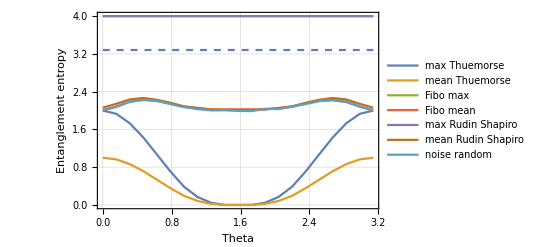

```mathematica
Show[ListLinePlot[{Etmmax,Etmmean,Efibomax,Efibomean,Ersmax,Ersmean,Efitvals8n},PlotLegends->{Thuemorse max,Thuemorse mean,Fibo max, Fibo mean, Rudin Shapiro max, Rudin Shapiro mean, random noise},PlotTheme->"Detailed",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Theta],None}},LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotRange->All],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],PlotRange->All]
```

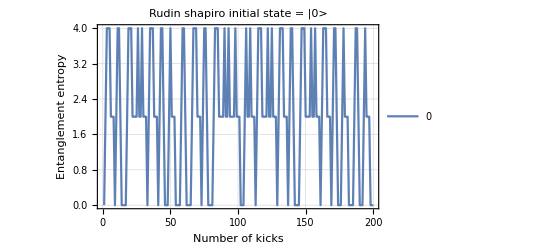

```mathematica
ListLinePlot[Ersn[[1]],PlotTheme->"Detailed",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotLabel->"Rudin shapiro initial state = |0>",PlotLegends->{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"}, PlotRange->All]
```

## CC correct dt = pi/8

#### data

```mathematica
Ersc = Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/Ecrudin8.dat"]];
```

### Plotting

```mathematica
Ecrsn=Table[Drop[Drop[Ersc,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Ecrsmax=Table[{0.05*(n-1)*Pi,Max[Ecrsn[[n]]]},{n,1,21}];
```

```mathematica
Ecrsmean=Table[{0.05 (n-1) Pi,Mean[Ecrsn[[n]]]},{n,1,21}];
```

```mathematica
Show[ListLinePlot[{Ecrsmax,Ecrsmean,Etmcmax,Etmcmean,Ecfibomax,Ecfibomean,Efitvals8n,entropymean},PlotLegends->{Rudin max,Rudin mean, TM max, TM mean, Fibo max ,Fibo mean,random noise, "mean when dt =0" },PlotTheme->"Detailed",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Theta],None}},LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotRange->All],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],PlotRange->All]
```

$Aborted

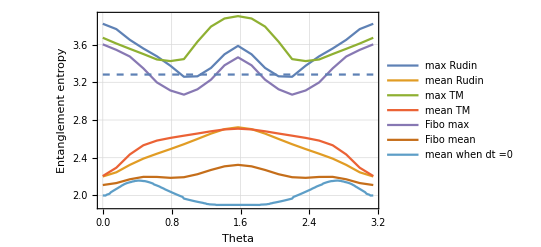

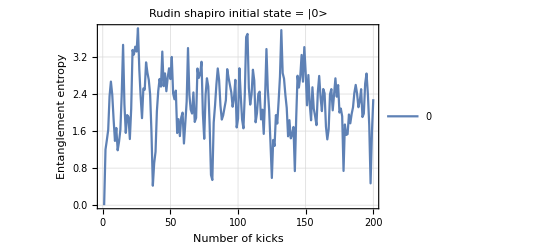

```mathematica
ListLinePlot[Ecrsn[[1]],PlotTheme->"Detailed",FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotLabel->"Rudin shapiro initial state = |0> ",PlotLegends->{"0 ","0.05 Pi","0.1 Pi","0.15 Pi","0.2 Pi","0.25 Pi","0.3 Pi","0.35 Pi","0.4 Pi","0.45 Pi","0.5 Pi"}, PlotRange->All]
```

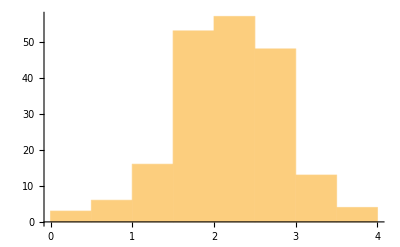
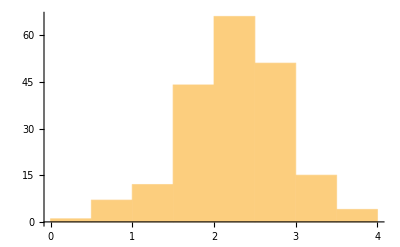
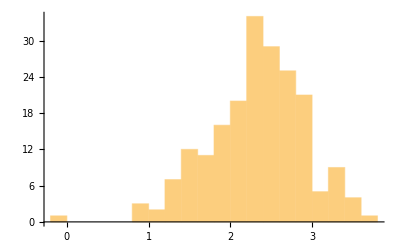
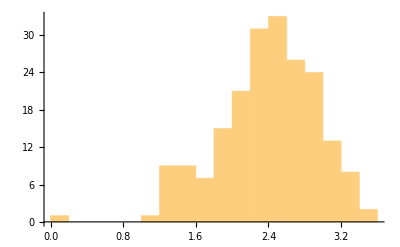
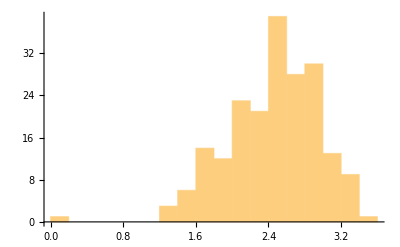
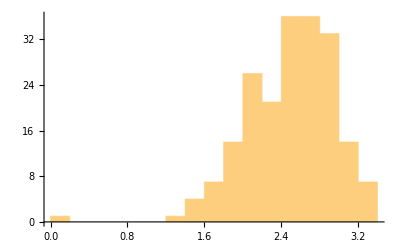
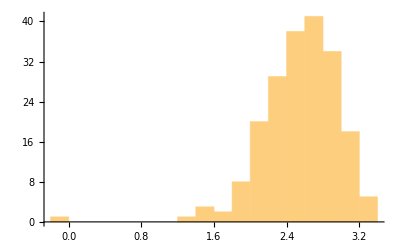
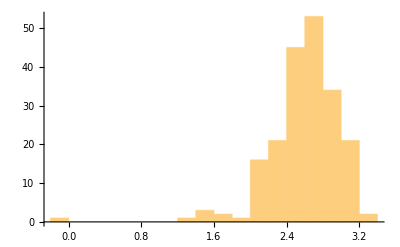

```mathematica
Table[Histogram[Ecrsn[[i]]],{i,1,10}]
```

```mathematica
c
```

c

## dt = pi/8

#### data

```mathematica
Tabl*10^[RudinShapiro[n],{n,0,200}]
```

```mathematica
rd={-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.398404964790534777*10^+00,2.398404964790533889*10^+00,2.398404964790534777*10^+00,2.769031713829399166*10^+00,2.769031713829400054*10^+00,2.769031713829398722*10^+00,2.714859631909449789*10^+00,1.435539529221185218*10^+00,2.233308640386463040*10^+00,2.233308640386463040*10^+00,1.435539529221186106*10^+00,2.714859631909444904*10^+00,2.714859631909446680*10^+00,2.714859631909446680*10^+00,2.714859631909445348*10^+00,1.435539529221186772*10^+00,2.233308640386460375*10^+00,2.233308640386461263*10^+00,2.233308640386461263*10^+00,7.718119272934460540*10^-01,7.718119272934463870*10^-01,7.718119272934467201*10^-01,7.718119272934464981*10^-01,2.233308640386459931*10^+00,1.435539529221186106*10^+00,1.435539529221186772*10^+00,2.233308640386457711*10^+00,7.718119272934471642*10^-01,7.718119272934473862*10^-01,7.718119272934479413*10^-01,1.933919985966688682*10^+00,2.902430850435071541*10^+00,2.178579989840964348*10^+00,2.178579989840964348*10^+00,2.178579989840963904*10^+00,2.433453312579537453*10^+00,2.433453312579539229*10^+00,2.433453312579537009*10^+00,1.400990072477377391*10^+00,2.679406902378255406*10^+00,1.722609701733388565*10^+00,1.722609701733388343*10^+00,2.679406902378254518*10^+00,1.400990072477376724*10^+00,1.400990072477377169*10^+00,1.400990072477376724*10^+00,2.433453312579533900*10^+00,2.178579989840961240*10^+00,2.902430850435062215*10^+00,2.902430850435062215*10^+00,2.902430850435061771*10^+00,1.933919985966685351*10^+00,1.933919985966685129*10^+00,1.933919985966685129*10^+00,1.933919985966684463*10^+00,2.902430850435059106*10^+00,2.178579989840959463*10^+00,2.178579989840959907*10^+00,2.902430850435057330*10^+00,1.933919985966683797*10^+00,1.933919985966683797*10^+00,1.933919985966683797*10^+00,1.933919985966684241*10^+00,2.902430850435057774*10^+00,2.178579989840958575*10^+00,2.178579989840958575*10^+00,2.178579989840957687*10^+00,2.433453312579526795*10^+00,2.433453312579526795*10^+00,2.433453312579525907*10^+00,1.400990072477377835*10^+00,2.679406902378242528*10^+00,1.722609701733385679*10^+00,1.722609701733385235*10^+00,2.679406902378241639*10^+00,1.400990072477378501*10^+00,1.400990072477378945*10^+00,1.400990072477378945*10^+00,1.400990072477379389*10^+00,2.679406902378239863*10^+00,1.722609701733384124*10^+00,1.722609701733384346*10^+00,1.722609701733383680*10^+00,1.415230676244290109*10^+00,1.415230676244290109*10^+00,1.415230676244290109*10^+00,1.415230676244290109*10^+00,1.722609701733384124*10^+00,2.679406902378235866*10^+00,2.679406902378235866*10^+00,1.722609701733383014*10^+00,1.415230676244289887*10^+00,1.415230676244289665*10^+00,1.415230676244289887*10^+00,1.415230676244290331*10^+00,1.722609701733383014*10^+00,2.679406902378234534*10^+00,2.679406902378232758*10^+00,2.679406902378233202*10^+00,1.400990072477381165*10^+00,1.400990072477381165*10^+00,1.400990072477381609*10^+00,2.433453312579512584*10^+00,2.178579989840950581*10^+00,2.902430850435035126*10^+00,2.902430850435035570*10^+00,2.178579989840949693*10^+00,2.433453312579509031*10^+00,2.433453312579508143*10^+00,2.433453312579507255*10^+00,1.400990072477382498*10^+00,2.679406902378224764*10^+00,1.722609701733380350*10^+00,1.722609701733380572*10^+00,1.722609701733380350*10^+00,1.415230676244289221*10^+00,1.415230676244289221*10^+00,1.415230676244289221*10^+00,1.415230676244289443*10^+00,1.722609701733379683*10^+00,2.679406902378223432*10^+00,2.679406902378222988*10^+00,1.722609701733379239*10^+00,1.415230676244288777*10^+00,1.415230676244288777*10^+00,1.415230676244288999*10^+00,2.673177896994376468*10^+00,1.387353866375297340*10^+00,2.575570761327266922*10^+00,2.575570761327266034*10^+00,2.575570761327267366*10^+00,2.218833447415865301*10^+00,2.218833447415864857*10^+00,2.218833447415864857*10^+00,2.702570864545668083*10^+00,2.092037360349433772*10^+00,4.968739972006174788*10^-01,4.968739972006175898*10^-01,2.092037360349433328*10^+00,2.702570864545665419*10^+00,2.702570864545664531*10^+00,2.702570864545665419*10^+00,2.702570864545665419*10^+00,2.092037360349432884*10^+00,4.968739972006189221*10^-01,4.968739972006189221*10^-01,4.968739972006195327*10^-01,2.198464746884048360*10^+00,2.198464746884048360*10^+00,2.198464746884048360*10^+00,2.198464746884047472*10^+00,4.968739972006215311*10^-01,2.092037360349430664*10^+00,2.092037360349430664*10^+00,4.968739972006216976*10^-01,2.198464746884045695*10^+00,2.198464746884046583*10^+00,2.198464746884045695*10^+00,1.826770023126994102*10^+00,2.925662522169257151*10^+00,2.605726898388087687*10^+00,2.605726898388087687*10^+00,2.605726898388088131*10^+00,2.007194037888679894*10^+00,2.007194037888680782*10^+00,2.007194037888680338*10^+00,1.999254061534527560*10^+00,1.844735960542518149*10^-01,1.999421107032012035*10^+00,1.999421107032012035*10^+00,1.844735960542540076*10^-01,1.999254061534526006*10^+00,1.999254061534525562*10^+00,1.999254061534525562*10^+00,2.007194037888677673*10^+00,2.605726898388081025*10^+00,2.925662522169246937*10^+00,2.925662522169245605*10^+00,2.925662522169246937*10^+00,1.826770023126991882*10^+00,1.826770023126991438*10^+00,1.826770023126992104*10^+00,1.826770023126991216*10^+00,2.925662522169243829*10^+00,2.605726898388077917*10^+00,2.605726898388077473*10^+00,2.925662522169242052*10^+00,1.826770023126990328*10^+00,1.826770023126990328*10^+00,1.826770023126990550*10^+00,2.198464746884036813*10^+00,4.968739972006336325*10^-01,2.092037360349422670*10^+00,2.092037360349421782*10^+00,2.092037360349423114*10^+00,2.702570864545644103*10^+00,2.702570864545643214*10^+00,2.702570864545643214*10^+00,2.722912528242654327*10^-14,1.964767092222882150*10^+00,2.355557808075303239*10^+00,2.355557808074924875*10^+00,2.355557808075303239*10^+00,2.744238183133894449*10^+00,2.744238183134098286*10^+00,2.744238183133894005*10^+00,2.811340969164806580*10^+00,1.667726355646765635*10^+00,2.398681502270943788*10^+00,2.398681502271174271*10^+00,1.667726355646516279*10^+00,2.811340969164802583*10^+00,2.811340969164802139*10^+00,2.811340969164803028*10^+00,2.811340969164801695*10^+00,1.667726355646766523*10^+00,2.398681502270941124*10^+00,2.398681502271171162*10^+00,2.398681502270940680*10^+00,1.071180964015251424*10^+00,1.071180964015251202*10^+00,1.071180964015251647*10^+00,1.071180964015251424*10^+00,2.398681502271171162*10^+00,1.667726355646517167*10^+00,1.667726355646766745*10^+00,2.398681502270938015*10^+00,1.071180964015252091*10^+00,1.071180964015252091*10^+00,1.071180964015252535*10^+00,2.172068796354834852*10^+00,2.929705051907824931*10^+00,2.191760201592816149*10^+00,2.191760201592816149*10^+00,2.191760201592815704*10^+00,2.414372968161970334*10^+00,2.414372968161970334*10^+00,2.414372968161970334*10^+00,1.302914787423258280*10^+00,2.571450518127324614*10^+00,1.782829949235794409*10^+00,1.782829949235794631*10^+00,2.571450518127324614*10^+00,1.302914787423210319*10^+00,1.302914787423258058*10^+00,1.302914787423210985*10^+00,2.414372968161965005*10^+00,2.191760201592812152*10^+00,2.929705051907814273*10^+00,2.929705051907814273*10^+00,2.929705051907815161*10^+00,2.172068796354829523*10^+00,2.172068796354829967*10^+00,2.172068796354829079*10^+00,2.172068796354829079*10^+00,2.929705051907811608*10^+00,2.191760201592810375*10^+00,2.191760201592809487*10^+00,2.929705051907811608*10^+00,2.172068796354828635*10^+00,2.172068796354828191*10^+00,2.172068796354827747*10^+00,2.172068796354828191*10^+00,2.929705051907809832*10^+00,2.191760201592808599*10^+00,2.191760201592809043*10^+00,2.191760201592808599*10^+00,2.414372968161957900*10^+00,2.414372968161958344*10^+00,2.414372968161957456*10^+00,1.302914787423260723*10^+00,2.571450518127312179*10^+00,1.782829949235790190*10^+00,1.782829949235790634*10^+00,2.571450518127312179*10^+00,1.302914787423214094*10^+00,1.302914787423261611*10^+00,1.302914787423213649*10^+00,1.302914787423262055*10^+00,2.571450518127309515*10^+00,1.782829949235788858*10^+00,1.782829949235788636*10^+00,1.782829949235789524*10^+00,1.502596748356643142*10^+00,1.502596748356643364*10^+00,1.502596748356643364*10^+00,1.502596748356643364*10^+00,1.782829949235788636*10^+00,2.571450518127306850*10^+00,2.571450518127306850*10^+00,1.782829949235788192*10^+00,1.502596748356643808*10^+00,1.502596748356642475*10^+00,1.502596748356643142*10^+00,1.502596748356643364*10^+00,1.782829949235787748*10^+00,2.571450518127305074*10^+00,2.571450518127304186*10^+00,2.571450518127304186*10^+00,1.302914787423215870*10^+00,1.302914787423263832*10^+00,1.302914787423216314*10^+00,2.414372968161944133*10^+00,2.191760201592801494*10^+00,2.929705051907787183*10^+00,2.929705051907788071*10^+00,2.191760201592801494*10^+00,2.414372968161941024*10^+00,2.414372968161941024*10^+00,2.414372968161941913*10^+00,1.302914787423265608*10^+00,2.571450518127296192*10^+00,1.782829949235783751*10^+00,1.782829949235783751*10^+00,1.782829949235785083*10^+00,1.502596748356642253*10^+00,1.502596748356641587*10^+00,1.502596748356642697*10^+00,1.502596748356642919*10^+00,1.782829949235783751*10^+00,2.571450518127293527*10^+00,2.571450518127293527*10^+00,1.782829949235783307*10^+00,1.502596748356641587*10^+00,1.502596748356642031*10^+00,1.502596748356641809*10^+00,2.728027574034631364*10^+00,1.646281467842358737*10^+00,2.670629339484541287*10^+00,2.670629339485885545*10^+00,2.670629339484542175*10^+00,2.344023947517617223*10^+00,2.344023947517616335*10^+00,2.344023947517616335*10^+00,2.740456726521895536*10^+00,2.192067905375441050*10^+00,7.207769157003671712*10^-01,7.207769157003671712*10^-01,2.192067905375440162*10^+00,2.740456726521895092*10^+00,2.740456726521893760*10^+00,2.740456726521893760*10^+00,2.740456726521894204*10^+00,2.192067905375439718*10^+00,7.207769157003683924*10^-01,7.207769157003685034*10^-01,7.207769157003691696*10^-01,2.249471107484183996*10^+00,2.249471107484183996*10^+00,2.249471107484182664*10^+00,2.249471107484183108*10^+00,7.207769157003709459*10^-01,2.192067905375436609*10^+00,2.192067905375436609*10^+00,7.207769157003719451*10^-01,2.249471107484181776*10^+00,2.249471107484181331*10^+00,2.249471107484181331*10^+00,1.860487923632872409*10^+00,2.959122598268919546*10^+00,2.628023141174868460*10^+00,2.628023141174868016*10^+00,2.628023141174868460*10^+00,2.060785606042940810*10^+00,2.060785606042941254*10^+00,2.060785606042940810*10^+00,2.192284566264760315*10^+00,5.196597729301660751*10^-01,2.160692085628590053*10^+00,2.160692085627428316*10^+00,5.196597729300829194*10^-01,2.192284566264758983*10^+00,2.192284566264758094*10^+00,2.192284566264758539*10^+00,2.060785606042939477*10^+00,2.628023141174861799*10^+00,2.959122598268684179*10^+00,2.959122598268910664*10^+00,2.959122598268681514*10^+00,1.860487923633680207*10^+00,1.860487923632869522*10^+00,1.860487923633679763*10^+00,1.860487923632869300*10^+00,2.959122598268908000*10^+00,2.628023141174860022*10^+00,2.628023141174859578*10^+00,2.959122598268677962*10^+00,1.860487923633679097*10^+00,1.860487923632869078*10^+00,1.860487923633679319*10^+00,2.249471107484171117*10^+00,7.207769157003804938*10^-01,2.192067905375425507*10^+00,2.192067905375425507*10^+00,2.192067905375425507*10^+00,2.740456726521873332*10^+00,2.740456726521873776*10^+00,2.740456726521873332*10^+00,-9.610279511444755881*10^-16,1.863352578568376661*10^+00,2.238062942591866555*10^+00,2.238062942591866555*10^+00,2.238062942591866555*10^+00,2.681853118328297203*10^+00,2.681853118328296315*10^+00,2.681853118328295871*10^+00,2.991904535099856766*10^+00,2.075972682423257165*10^+00,2.598116832876621096*10^+00,2.598116832876620208*10^+00,2.075972682423256721*10^+00,2.991904535099853213*10^+00,2.991904535099851881*10^+00,2.991904535099851437*10^+00,2.991904535099850992*10^+00,2.075972682423256721*10^+00,2.598116832876616655*10^+00,2.598116832876616655*10^+00,2.598116832876617543*10^+00,1.632724986113660348*10^+00,1.632724986113660570*10^+00,1.632724986113661014*10^+00,1.632724986113660570*10^+00,2.598116832876615767*10^+00,2.075972682423254945*10^+00,2.075972682423254945*10^+00,2.598116832876614435*10^+00,1.632724986113660126*10^+00,1.632724986113660570*10^+00,1.632724986113660126*10^+00,2.526215665702665980*10^+00,2.997437025838650904*10^+00,2.263529622832971100*10^+00,2.263529622832971100*10^+00,2.263529622832970656*10^+00,2.377129360274349068*10^+00,2.377129360274349956*10^+00,2.377129360274349068*10^+00,1.102944359078667169*10^+00,2.295754290086527760*10^+00,1.878608384020148847*10^+00,1.878608384020148181*10^+00,2.295754290086528648*10^+00,1.102944359078666947*10^+00,1.102944359078667613*10^+00,1.102944359078667835*10^+00,2.377129360274345515*10^+00,2.263529622832968435*10^+00,2.997437025838640245*10^+00,2.997437025838642466*10^+00,2.997437025838641134*10^+00,2.526215665702658875*10^+00,2.526215665702658875*10^+00,2.526215665702658875*10^+00,2.526215665702657986*10^+00,2.997437025838639801*10^+00,2.263529622832964883*10^+00,2.263529622832965771*10^+00,2.997437025838636693*10^+00,2.526215665702656654*10^+00,2.526215665702655766*10^+00,2.526215665702656210*10^+00,2.526215665702655322*10^+00,2.997437025838636249*10^+00,2.263529622832963994*10^+00,2.263529622832963994*10^+00,2.263529622832963550*10^+00,2.377129360274337966*10^+00,2.377129360274338410*10^+00,2.377129360274337078*10^+00,1.102944359078671166*10^+00,2.295754290086518434*10^+00,1.878608384020142630*10^+00,1.878608384020143074*10^+00,2.295754290086517990*10^+00,1.102944359078672498*10^+00,1.102944359078672054*10^+00,1.102944359078672498*10^+00,1.102944359078671610*10^+00,2.295754290086515770*10^+00,1.878608384020142186*10^+00,1.878608384020141742*10^+00,1.878608384020141742*10^+00,1.722495489776571187*10^+00,1.722495489776570965*10^+00,1.722495489776571187*10^+00,1.722495489776571409*10^+00,1.878608384020141520*10^+00,2.295754290086512661*10^+00,2.295754290086512661*10^+00,1.878608384020140853*10^+00,1.722495489776570299*10^+00,1.722495489776569855*10^+00,1.722495489776570299*10^+00,1.722495489776570299*10^+00,1.878608384020140631*10^+00,2.295754290086512661*10^+00,2.295754290086510885*10^+00,2.295754290086511773*10^+00,1.102944359078676051*10^+00,1.102944359078675829*10^+00,1.102944359078675829*10^+00,2.377129360274325531*10^+00,2.263529622832954225*10^+00,2.997437025838614044*10^+00,2.997437025838614044*10^+00,2.263529622832953780*10^+00,2.377129360274323311*10^+00,2.377129360274322867*10^+00,2.377129360274323755*10^+00,1.102944359078677383*10^+00,2.295754290086506444*10^+00,1.878608384020137301*10^+00,1.878608384020138189*10^+00,1.878608384020137523*10^+00,1.722495489776568300*10^+00,1.722495489776568078*10^+00,1.722495489776568078*10^+00,1.722495489776568300*10^+00,1.878608384020137301*10^+00,2.295754290086503335*10^+00,2.295754290086503779*10^+00,1.878608384020135968*10^+00,1.722495489776567634*10^+00,1.722495489776567634*10^+00,1.722495489776568078*10^+00,2.801720694928233613*10^+00,2.095855057099355712*10^+00,2.839216383326240045*10^+00,2.839216383326239601*10^+00,2.839216383326239157*10^+00,2.602915257911862401*10^+00,2.602915257911863289*10^+00,2.602915257911862845*10^+00,2.791592860933668430*10^+00,2.401845200890107890*10^+00,1.193418560861601030*10^+00,1.193418560861601918*10^+00,2.401845200890105225*10^+00,2.791592860933666653*10^+00,2.791592860933666209*10^+00,2.791592860933666209*10^+00,2.791592860933665321*10^+00,2.401845200890104337*10^+00,1.193418560861602362*10^+00,1.193418560861602140*10^+00,1.193418560861602362*10^+00,2.355302835095985703*10^+00,2.355302835095985259*10^+00,2.355302835095985703*10^+00,2.355302835095985259*10^+00,1.193418560861603472*10^+00,2.401845200890101673*10^+00,2.401845200890100784*10^+00,1.193418560861604139*10^+00,2.355302835095982594*10^+00,2.355302835095982594*10^+00,2.355302835095983482*10^+00,1.933735018467714228*10^+00,3.018539575534501918*10^+00,2.708246931196843565*10^+00,2.708246931196843121*10^+00,2.708246931196842677*10^+00,2.271494167076577142*10^+00,2.271494167076577586*10^+00,2.271494167076577586*10^+00,2.491918851082430386*10^+00,1.143353440859400605*10^+00,2.372469258848916240*10^+00,2.372469258848915352*10^+00,1.143353440859401715*10^+00,2.491918851082427722*10^+00,2.491918851082427722*10^+00,2.491918851082427722*10^+00,2.271494167076574922*10^+00,2.708246931196836904*10^+00,3.018539575534492148*10^+00,3.018539575534492148*10^+00,3.018539575534492592*10^+00,1.933735018467709788*10^+00,1.933735018467710010*10^+00,1.933735018467710676*10^+00,1.933735018467710232*10^+00,3.018539575534489483*10^+00,2.708246931196834240*10^+00,2.708246931196833351*10^+00,3.018539575534487707*10^+00,1.933735018467709565*10^+00,1.933735018467709121*10^+00,1.933735018467709121*10^+00,2.355302835095971936*10^+00,1.193418560861608135*10^+00,2.401845200890088350*10^+00,2.401845200890087462*10^+00,2.401845200890088350*10^+00,2.791592860933643117*10^+00,2.791592860933641340*10^+00,2.791592860933642228*10^+00,9.610279511444749964*10^-16,1.707978246994109384*10^+00,2.053926717850639516*10^+00,2.053926717850639960*10^+00,2.053926717850639516*10^+00,2.603498229152986898*10^+00,2.603498229152986454*10^+00,2.603498229152986010*10^+00,3.125639763649246561*10^+00,2.376050243634326264*10^+00,2.641579586264520163*10^+00,2.641579586264521051*10^+00,2.376050243634326264*10^+00,3.125639763649242564*10^+00,3.125639763649242564*10^+00,3.125639763649243008*10^+00,3.125639763649241676*10^+00,2.376050243634324488*10^+00,2.641579586264517054*10^+00,2.641579586264516610*10^+00,2.641579586264516610*10^+00,2.134583599413069521*10^+00,2.134583599413069521*10^+00,2.134583599413069521*10^+00,2.134583599413069521*10^+00,2.641579586264516166*10^+00,2.376050243634322712*10^+00,2.376050243634323156*10^+00,2.641579586264515278*10^+00,2.134583599413068633*10^+00,2.134583599413068633*10^+00,2.134583599413068633*10^+00,2.816933284158663398*10^+00,3.056722091243476047*10^+00,2.286056092729754408*10^+00,2.286056092729753964*10^+00,2.286056092729754852*10^+00,2.278572194332086909*10^+00,2.278572194332086465*10^+00,2.278572194332086465*10^+00,9.904075577051056900*10^-01,2.000185922753511480*10^+00,1.930705438124643569*10^+00,1.930705438124644235*10^+00,2.000185922753512369*10^+00,9.904075577051065782*10^-01,9.904075577051065782*10^-01,9.904075577051059120*10^-01,2.278572194332083356*10^+00,2.286056092729751299*10^+00,3.056722091243466721*10^+00,3.056722091243464945*10^+00,3.056722091243465833*10^+00,2.816933284158653628*10^+00,2.816933284158653628*10^+00,2.816933284158653183*10^+00,2.816933284158653628*10^+00,3.056722091243464057*10^+00,2.286056092729749079*10^+00,2.286056092729748190*10^+00,3.056722091243461836*10^+00,2.816933284158651851*10^+00,2.816933284158650963*10^+00,2.816933284158650963*10^+00,2.816933284158651407*10^+00,3.056722091243460504*10^+00,2.286056092729747302*10^+00,2.286056092729747302*10^+00,2.286056092729746858*10^+00,2.278572194332079803*10^+00,2.278572194332078915*10^+00,2.278572194332078915*10^+00,9.904075577051107970*10^-01,2.000185922753507040*10^+00,1.930705438124640461*10^+00,1.930705438124640461*10^+00,2.000185922753507484*10^+00,9.904075577051123513*10^-01,9.904075577051122403*10^-01,9.904075577051113521*10^-01,9.904075577051117962*10^-01,2.000185922753505707*10^+00,1.930705438124638906*10^+00,1.930705438124638684*10^+00,1.930705438124638462*10^+00,1.948233473225385870*10^+00,1.948233473225386980*10^+00,1.948233473225385648*10^+00,1.948233473225386092*10^+00,1.930705438124638018*10^+00,2.000185922753504375*10^+00,2.000185922753503931*10^+00,1.930705438124637574*10^+00,1.948233473225385426*10^+00,1.948233473225385204*10^+00,1.948233473225384316*10^+00,1.948233473225385426*10^+00,1.930705438124637574*10^+00,2.000185922753502155*10^+00,2.000185922753503043*10^+00,2.000185922753502599*10^+00,9.904075577051152379*10^-01,9.904075577051160151*10^-01,9.904075577051157930*10^-01,2.278572194332069145*10^+00,2.286056092729738420*10^+00,3.056722091243440520*10^+00,3.056722091243440076*10^+00,2.286056092729738420*10^+00,2.278572194332066481*10^+00,2.278572194332066481*10^+00,2.278572194332066037*10^+00,9.904075577051167922*10^-01,2.000185922753499490*10^+00,1.930705438124635354*10^+00,1.930705438124635576*10^+00,1.930705438124634910*10^+00,1.948233473225382983*10^+00,1.948233473225381429*10^+00,1.948233473225382539*10^+00,1.948233473225382095*10^+00,1.930705438124633577*10^+00,2.000185922753498602*10^+00,2.000185922753498602*10^+00,1.930705438124633799*10^+00,1.948233473225381651*10^+00,1.948233473225381207*10^+00,1.948233473225381429*10^+00,2.816897899413786988*10^+00,2.414266138995117661*10^+00,2.903268109365765959*10^+00,2.903268109365765515*10^+00,2.903268109365765071*10^+00,2.830408313579926727*10^+00,2.830408313579926727*10^+00,2.830408313579925839*10^+00,2.807115355318221539*10^+00,2.568995254771888614*10^+00,1.625545488810949291*10^+00,1.625545488810948846*10^+00,2.568995254771885950*10^+00,2.807115355318219763*10^+00,2.807115355318218430*10^+00,2.807115355318219319*10^+00,2.807115355318218430*10^+00,2.568995254771885062*10^+00,1.625545488810949069*10^+00,1.625545488810949069*10^+00,1.625545488810948846*10^+00,2.402720294259156120*10^+00,2.402720294259157008*10^+00,2.402720294259157008*10^+00,2.402720294259156564*10^+00,1.625545488810948846*10^+00,2.568995254771883285*10^+00,2.568995254771881953*10^+00,1.625545488810949291*10^+00,2.402720294259153455*10^+00,2.402720294259154343*10^+00,2.402720294259153899*10^+00,1.979675624904989828*10^+00,3.014064764783102035*10^+00,2.800113059379693681*10^+00,2.800113059379693237*10^+00,2.800113059379692348*10^+00,2.510538736403411519*10^+00,2.510538736403410631*10^+00,2.510538736403411519*10^+00,2.660780916184678269*10^+00,1.684551608570389769*10^+00,2.492209445488382080*10^+00,2.492209445488381636*10^+00,1.684551608570390213*10^+00,2.660780916184675604*10^+00,2.660780916184674272*10^+00,2.660780916184674272*10^+00,2.510538736403408411*10^+00,2.800113059379686575*10^+00,3.014064764783090933*10^+00,3.014064764783090489*10^+00,3.014064764783091377*10^+00,1.979675624904988052*10^+00,1.979675624904987608*10^+00,1.979675624904987385*10^+00,1.979675624904987608*10^+00,3.014064764783089601*10^+00,2.800113059379683023*10^+00,2.800113059379683467*10^+00,3.014064764783088268*10^+00,1.979675624904987163*10^+00,1.979675624904986941*10^+00,1.979675624904987608*10^+00,2.402720294259143685*10^+00,1.625545488810949735*10^+00,2.568995254771868186*10^+00,2.568995254771867742*10^+00,2.568995254771868186*10^+00,2.807115355318195782*10^+00,2.807115355318196226*10^+00,2.807115355318195782*10^+00,4.805139755722374982*10^-16,1.516990580024020652*10^+00,1.878024604037902279*10^+00,1.878024604037900946*10^+00,1.878024604037902057*10^+00,2.511525742351230051*10^+00,2.511525742351229162*10^+00,2.511525742351228718*10^+00,3.152157196449888676*10^+00,2.507489025168848862*10^+00,2.529218200248953163*10^+00,2.529218200248953163*10^+00,2.507489025168848418*10^+00,3.152157196449885568*10^+00,3.152157196449885568*10^+00,3.152157196449885124*10^+00,3.152157196449885124*10^+00,2.507489025168846641*10^+00,2.529218200248949611*10^+00,2.529218200248949611*10^+00,2.529218200248950055*10^+00,2.432291071226570178*10^+00,2.432291071226571066*10^+00,2.432291071226570622*10^+00,2.432291071226571066*10^+00,2.529218200248948278*10^+00,2.507489025168845309*10^+00,2.507489025168844421*10^+00,2.529218200248946502*10^+00,2.432291071226568846*10^+00,2.432291071226568846*10^+00,2.432291071226569290*10^+00,2.926581176779572413*10^+00,3.028941037561028615*10^+00,2.200355127966227897*10^+00,2.200355127966228341*10^+00,2.200355127966228341*10^+00,2.079797024447525011*10^+00,2.079797024447525455*10^+00,2.079797024447525455*10^+00,9.971972080410580475*10^-01,1.761423552734428633*10^+00,1.838223221639128546*10^+00,1.838223221639128990*10^+00,1.761423552734429299*10^+00,9.971972080410589356*10^-01,9.971972080410593797*10^-01,9.971972080410593797*10^-01,2.079797024447522347*10^+00,2.200355127966225233*10^+00,3.028941037561019289*10^+00,3.028941037561020622*10^+00,3.028941037561019733*10^+00,2.926581176779563531*10^+00,2.926581176779563975*10^+00,2.926581176779563975*10^+00,2.926581176779563087*10^+00,3.028941037561018401*10^+00,2.200355127966223900*10^+00,2.200355127966222124*10^+00,3.028941037561015293*10^+00,2.926581176779561311*10^+00,2.926581176779560423*10^+00,2.926581176779560423*10^+00,2.926581176779560423*10^+00,3.028941037561015293*10^+00,2.200355127966221680*10^+00,2.200355127966222568*10^+00,2.200355127966221680*10^+00,2.079797024447519682*10^+00,2.079797024447518794*10^+00,2.079797024447518794*10^+00,9.971972080410622663*10^-01,1.761423552734425746*10^+00,1.838223221639124993*10^+00,1.838223221639125438*10^+00,1.761423552734425080*10^+00,9.971972080410630435*10^-01,9.971972080410637096*10^-01,9.971972080410634875*10^-01,9.971972080410634875*10^-01,1.761423552734425524*10^+00,1.838223221639125438*10^+00,1.838223221639124771*10^+00,1.838223221639124105*10^+00,2.081839380131904171*10^+00,2.081839380131904615*10^+00,2.081839380131904615*10^+00,2.081839380131904171*10^+00,1.838223221639123883*10^+00,1.761423552734424414*10^+00,1.761423552734424414*10^+00,1.838223221639124105*10^+00,2.081839380131902395*10^+00,2.081839380131902839*10^+00,2.081839380131903283*10^+00,2.081839380131902839*10^+00,1.838223221639122773*10^+00,1.761423552734424192*10^+00,1.761423552734423970*10^+00,1.761423552734423525*10^+00,9.971972080410684836*10^-01,9.971972080410672623*10^-01,9.971972080410675954*10^-01,2.079797024447513465*10^+00,2.200355127966215463*10^+00,3.028941037560995753*10^+00,3.028941037560995753*10^+00,2.200355127966214575*10^+00,2.079797024447510356*10^+00,2.079797024447512133*10^+00,2.079797024447510800*10^+00,9.971972080410694828*10^-01,1.761423552734420417*10^+00,1.838223221639120997*10^+00,1.838223221639120553*10^+00,1.838223221639121885*10^+00,2.081839380131898842*10^+00,2.081839380131899730*10^+00,2.081839380131898398*10^+00,2.081839380131897954*10^+00,1.838223221639120553*10^+00,1.761423552734420195*10^+00,1.761423552734421083*10^+00,1.838223221639120331*10^+00,2.081839380131897510*10^+00,2.081839380131897510*10^+00,2.081839380131897954*10^+00,2.755063284016517677*10^+00,2.510653708869870826*10^+00,2.836396490340806764*10^+00,2.836396490340805432*10^+00,2.836396490340806320*10^+00,2.940666757587684810*10^+00,2.940666757587684810*10^+00,2.940666757587683922*10^+00,2.716972545937958117*10^+00,2.588303402223596006*10^+00,1.867189846081195315*10^+00,1.867189846081195093*10^+00,2.588303402223594230*10^+00,2.716972545937957229*10^+00,2.716972545937955896*10^+00,2.716972545937956340*10^+00,2.716972545937955452*10^+00,2.588303402223593785*10^+00,1.867189846081194204*10^+00,1.867189846081193538*10^+00,1.867189846081193760*10^+00,2.274348848825310743*10^+00,2.274348848825310743*10^+00,2.274348848825310743*10^+00,2.274348848825310299*10^+00,1.867189846081193316*10^+00,2.588303402223591121*10^+00,2.588303402223589789*10^+00,1.867189846081192428*10^+00,2.274348848825308522*10^+00,2.274348848825308522*10^+00,2.274348848825308522*10^+00,1.924792583148881242*10^+00,2.872647493513322825*10^+00,2.797615230721177682*10^+00,2.797615230721176793*10^+00,2.797615230721177237*10^+00,2.659727878287114766*10^+00,2.659727878287114766*10^+00,2.659727878287114322*10^+00,2.645111356505907896*10^+00,1.984588295971577043*10^+00,2.510740874110356291*10^+00,2.510740874110356735*10^+00,1.984588295971577043*10^+00,2.645111356505904787*10^+00,2.645111356505904787*10^+00,2.645111356505904787*10^+00,2.659727878287111213*10^+00,2.797615230721170576*10^+00,2.872647493513315275*10^+00,2.872647493513314831*10^+00,2.872647493513314831*10^+00,1.924792583148877911*10^+00,1.924792583148878355*10^+00,1.924792583148878355*10^+00,1.924792583148878355*10^+00,2.872647493513313499*10^+00,2.797615230721168800*10^+00,2.797615230721168800*10^+00,2.872647493513312611*10^+00,1.924792583148877911*10^+00,1.924792583148877245*10^+00,1.924792583148877245*10^+00,2.274348848825300529*10^+00,1.867189846081188875*10^+00,2.588303402223576466*10^+00,2.588303402223575134*10^+00,2.588303402223576022*10^+00,2.716972545937937689*10^+00,2.716972545937937689*10^+00,2.716972545937937689*10^+00,3.203426503814917641*10^-16,1.312115125945429117*10^+00,1.677534864975295914*10^+00,1.677534864975296358*10^+00,1.677534864975296136*10^+00,2.369657556955557354*10^+00,2.369657556955557354*10^+00,2.369657556955556910*10^+00,3.020256060352169314*10^+00,2.458271301135006581*10^+00,2.307731872548244745*10^+00,2.307731872548244745*10^+00,2.458271301135006581*10^+00,3.020256060352166205*10^+00,3.020256060352166649*10^+00,3.020256060352166649*10^+00,3.020256060352165761*10^+00,2.458271301135004805*10^+00,2.307731872548242524*10^+00,2.307731872548242080*10^+00,2.307731872548241636*10^+00,2.497532331910383263*10^+00,2.497532331910383263*10^+00,2.497532331910383263*10^+00,2.497532331910383263*10^+00,2.307731872548241192*10^+00,2.458271301135003029*10^+00,2.458271301135002140*10^+00,2.307731872548240304*10^+00,2.497532331910381931*10^+00,2.497532331910381487*10^+00,2.497532331910381487*10^+00,2.839951548896356481*10^+00,2.843994508297678969*10^+00,2.027256535589058828*10^+00,2.027256535589059716*10^+00,2.027256535589059272*10^+00,1.748123928794688142*10^+00,1.748123928794688586*10^+00,1.748123928794688364*10^+00,9.905528088831506706*10^-01,1.568767522915062607*10^+00,1.662931038207292822*10^+00,1.662931038207293266*10^+00,1.568767522915063495*10^+00,9.905528088831510036*10^-01,9.905528088831514477*10^-01,9.905528088831514477*10^-01,1.748123928794688364*10^+00,2.027256535589056607*10^+00,2.843994508297670532*10^+00,2.843994508297670087*10^+00,2.843994508297669643*10^+00,2.839951548896347600*10^+00,2.839951548896348044*10^+00,2.839951548896347155*10^+00,2.839951548896347155*10^+00,2.843994508297668311*10^+00,2.027256535589056163*10^+00,2.027256535589055719*10^+00,2.843994508297667423*10^+00,2.839951548896344935*10^+00,2.839951548896344935*10^+00,2.839951548896344935*10^+00,2.839951548896344935*10^+00,2.843994508297666091*10^+00,2.027256535589055275*10^+00,2.027256535589055719*10^+00,2.027256535589054831*10^+00,1.748123928794687920*10^+00,1.748123928794687254*10^+00,1.748123928794687032*10^+00,9.905528088831554445*10^-01,1.568767522915062163*10^+00,1.662931038207293044*10^+00,1.662931038207292156*10^+00,1.568767522915062163*10^+00,9.905528088831571099*10^-01,9.905528088831574429*10^-01,9.905528088831572209*10^-01,9.905528088831584421*10^-01,1.568767522915063051*10^+00,1.662931038207293488*10^+00,1.662931038207292600*10^+00,1.662931038207292600*10^+00,2.073477662701954216*10^+00,2.073477662701954216*10^+00,2.073477662701955104*10^+00,2.073477662701955104*10^+00,1.662931038207292822*10^+00,1.568767522915063495*10^+00,1.568767522915062607*10^+00,1.662931038207293044*10^+00,2.073477662701953772*10^+00,2.073477662701953328*10^+00,2.073477662701952884*10^+00,2.073477662701953328*10^+00,1.662931038207292378*10^+00,1.568767522915063495*10^+00,1.568767522915063495*10^+00,1.568767522915063273*10^+00,9.905528088831622169*10^-01,9.905528088831623279*10^-01,9.905528088831621059*10^-01,1.748123928794686144*10^+00,2.027256535589051722*10^+00,2.843994508297651436*10^+00,2.843994508297650992*10^+00,2.027256535589050834*10^+00,1.748123928794685700*10^+00,1.748123928794685700*10^+00,1.748123928794684812*10^+00,9.905528088831635491*10^-01,1.568767522915061718*10^+00,1.662931038207292822*10^+00,1.662931038207292156*10^+00,1.662931038207292378*10^+00,2.073477662701949775*10^+00,2.073477662701949775*10^+00,2.073477662701949775*10^+00,2.073477662701950219*10^+00,1.662931038207291490*10^+00,1.568767522915061274*10^+00,1.568767522915061940*10^+00,1.662931038207292822*10^+00,2.073477662701948887*10^+00,2.073477662701948443*10^+00,2.073477662701948887*10^+00,2.615622346266120779*10^+00,2.400588671670130125*10^+00,2.652849684634778438*10^+00,2.652849684634777550*10^+00,2.652849684634778438*10^+00,2.869998024899444999*10^+00,2.869998024899445888*10^+00,2.869998024899444555*10^+00,2.536965506288801464*10^+00,2.414806813441924938*10^+00,1.885533729746629694*10^+00,1.885533729746630138*10^+00,2.414806813441925382*10^+00,2.536965506288799688*10^+00,2.536965506288799688*10^+00,2.536965506288799688*10^+00,2.536965506288799244*10^+00,2.414806813441923161*10^+00,1.885533729746628806*10^+00,1.885533729746628584*10^+00,1.885533729746628584*10^+00,1.968395288285515132*10^+00,1.968395288285514466*10^+00,1.968395288285514022*10^+00,1.968395288285514244*10^+00,1.885533729746628584*10^+00,2.414806813441921385*10^+00,2.414806813441920497*10^+00,1.885533729746628140*10^+00,1.968395288285513356*10^+00,1.968395288285512912*10^+00,1.968395288285512912*10^+00,1.765872596966678643*10^+00,2.584761283874763116*10^+00,2.625831182486507487*10^+00,2.625831182486507487*10^+00,2.625831182486506599*10^+00,2.638941541843759175*10^+00,2.638941541843759175*10^+00,2.638941541843758731*10^+00,2.486058312497034795*10^+00,2.028142756565833871*10^+00,2.425108612280197029*10^+00,2.425108612280196141*10^+00,2.028142756565833427*10^+00,2.486058312497033462*10^+00,2.486058312497033462*10^+00,2.486058312497032574*10^+00,2.638941541843756067*10^+00,2.625831182486503046*10^+00,2.584761283874757787*10^+00,2.584761283874757787*10^+00,2.584761283874756899*10^+00,1.765872596966678643*10^+00,1.765872596966678643*10^+00,1.765872596966678643*10^+00,1.765872596966677532*10^+00,2.584761283874756010*10^+00,2.625831182486500381*10^+00,2.625831182486501270*10^+00,2.584761283874755122*10^+00,1.765872596966677532*10^+00,1.765872596966678199*10^+00,1.765872596966677310*10^+00,1.968395288285508915*10^+00,1.885533729746625031*10^+00,2.414806813441910283*10^+00,2.414806813441909839*10^+00,2.414806813441909839*10^+00,2.536965506288785477*10^+00,2.536965506288785477*10^+00,2.536965506288784589*10^+00,-9.610279511444755881*10^-16,1.115222582521595562*10^+00,1.489891986783104416*10^+00,1.489891986783104194*10^+00,1.489891986783104194*10^+00,2.167108989211501413*10^+00,2.167108989211501413*10^+00,2.167108989211500969*10^+00,2.744713410251427899*10^+00,2.256659447525552586*10^+00,2.080429277345416494*10^+00,2.080429277345415606*10^+00,2.256659447525551698*10^+00,2.744713410251425234*10^+00,2.744713410251425234*10^+00,2.744713410251425234*10^+00,2.744713410251424346*10^+00,2.256659447525550366*10^+00,2.080429277345414718*10^+00,2.080429277345414274*10^+00,2.080429277345414274*10^+00,2.358192298704766987*10^+00,2.358192298704766543*10^+00,2.358192298704766543*10^+00,2.358192298704766987*10^+00,2.080429277345413386*10^+00,2.256659447525549478*10^+00,2.256659447525549034*10^+00,2.080429277345412942*10^+00,2.358192298704765655*10^+00,2.358192298704766099*10^+00,2.358192298704764767*10^+00,2.590213607472487745*10^+00,2.495707233303613215*10^+00,1.780463975529722909*10^+00,1.780463975529722465*10^+00,1.780463975529722687*10^+00,1.335179889528441022*10^+00,1.335179889528440800*10^+00,1.335179889528441244*10^+00,9.013908910937118435*10^-01,1.378392807897333094*10^+00,1.446323300615059315*10^+00,1.446323300615059315*10^+00,1.378392807897333761*10^+00,9.013908910937146191*10^-01,9.013908910937141750*10^-01,9.013908910937149521*10^-01,1.335179889528442132*10^+00,1.780463975529721798*10^+00,2.495707233303609662*10^+00,2.495707233303608774*10^+00,2.495707233303609218*10^+00,2.590213607472481971*10^+00,2.590213607472481971*10^+00,2.590213607472481527*10^+00,2.590213607472481527*10^+00,2.495707233303607886*10^+00,1.780463975529722687*10^+00,1.780463975529722465*10^+00,2.495707233303606998*10^+00,2.590213607472480195*10^+00,2.590213607472480195*10^+00,2.590213607472480195*10^+00,2.590213607472479751*10^+00,2.495707233303606110*10^+00,1.780463975529721576*10^+00,1.780463975529721576*10^+00,1.780463975529721132*10^+00,1.335179889528444352*10^+00,1.335179889528444797*10^+00,1.335179889528445019*10^+00,9.013908910937199481*10^-01,1.378392807897335759*10^+00,1.446323300615061758*10^+00,1.446323300615061536*10^+00,1.378392807897336203*10^+00,9.013908910937213914*10^-01,9.013908910937218355*10^-01,9.013908910937219465*10^-01,9.013908910937219465*10^-01,1.378392807897335981*10^+00,1.446323300615062424*10^+00,1.446323300615063090*10^+00,1.446323300615063312*10^+00,1.941005180594023383*10^+00,1.941005180594024049*10^+00,1.941005180594023827*10^+00,1.941005180594024271*10^+00,1.446323300615062646*10^+00,1.378392807897337535*10^+00,1.378392807897337313*10^+00,1.446323300615063090*10^+00,1.941005180594023383*10^+00,1.941005180594023383*10^+00,1.941005180594022939*10^+00,1.941005180594024049*10^+00,1.446323300615063534*10^+00,1.378392807897338868*10^+00,1.378392807897338646*10^+00,1.378392807897339312*10^+00,9.013908910937284968*10^-01,9.013908910937274976*10^-01,9.013908910937282748*10^-01,1.335179889528448793*10^+00,1.780463975529720910*10^+00,2.495707233303596784*10^+00,2.495707233303595451*10^+00,1.780463975529720244*10^+00,1.335179889528448793*10^+00,1.335179889528448349*10^+00,1.335179889528449015*10^+00,9.013908910937294960*10^-01,1.378392807897338646*10^+00,1.446323300615064644*10^+00,1.446323300615065532*10^+00,1.446323300615065532*10^+00,1.941005180594020718*10^+00,1.941005180594020940*10^+00,1.941005180594020718*10^+00,1.941005180594020496*10^+00,1.446323300615064422*10^+00,1.378392807897339090*10^+00,1.378392807897339534*10^+00,1.446323300615065754*10^+00,1.941005180594020940*10^+00,1.941005180594020718*10^+00,1.941005180594020274*10^+00,2.414294484513147321*10^+00,2.184349417323243614*10^+00,2.384070749222608754*10^+00,2.384070749222609642*10^+00,2.384070749222608310*10^+00,2.637880883818752853*10^+00,2.637880883818753297*10^+00,2.637880883818753741*10^+00,2.289396623786271512*10^+00,2.085623327360657253*10^+00,1.719744381628938612*10^+00,1.719744381628938168*10^+00,2.085623327360656809*10^+00,2.289396623786271068*10^+00,2.289396623786270180*10^+00,2.289396623786269735*10^+00,2.289396623786269735*10^+00,2.085623327360656809*10^+00,1.719744381628937280*10^+00,1.719744381628937724*10^+00,1.719744381628937946*10^+00,1.552036966177985589*10^+00,1.552036966177985366*10^+00,1.552036966177985366*10^+00,1.552036966177985589*10^+00,1.719744381628936836*10^+00,2.085623327360654589*10^+00,2.085623327360654589*10^+00,1.719744381628936614*10^+00,1.552036966177985366*10^+00,1.552036966177985811*10^+00,1.552036966177985589*10^+00,1.515570493426457332*10^+00,2.199238490342870112*10^+00,2.324319052856413048*10^+00,2.324319052856413492*10^+00,2.324319052856413048*10^+00,2.449826159729997066*10^+00,2.449826159729997510*10^+00,2.449826159729997510*10^+00,2.238582626786225660*10^+00,1.889895461392103737*10^+00,2.239101090643877967*10^+00,2.239101090643878411*10^+00,1.889895461392103515*10^+00,2.238582626786224328*10^+00,2.238582626786223884*10^+00,2.238582626786223884*10^+00,2.449826159729995290*10^+00,2.324319052856410384*10^+00,2.199238490342868335*10^+00,2.199238490342867891*10^+00,2.199238490342866559*10^+00,1.515570493426457777*10^+00,1.515570493426457555*10^+00,1.515570493426457777*10^+00,1.515570493426457999*10^+00,2.199238490342866115*10^+00,2.324319052856409051*10^+00,2.324319052856409051*10^+00,2.199238490342866115*10^+00,1.515570493426458443*10^+00,1.515570493426458221*10^+00,1.515570493426458221*10^+00,1.552036966177986255*10^+00,1.719744381628935725*10^+00,2.085623327360648815*10^+00,2.085623327360648371*10^+00,2.085623327360648371*10^+00,2.289396623786261298*10^+00,2.289396623786261298*10^+00,2.289396623786261742*10^+00,-3.203426503814917641*10^-16,9.452589891428944124*10^-01,1.305103911544364781*10^+00,1.305103911544365891*10^+00,1.305103911544364337*10^+00,1.887993229853869970*10^+00,1.887993229853869970*10^+00,1.887993229853869082*10^+00,2.375019397043162783*10^+00,1.989251388745264304*10^+00,1.836783510896070393*10^+00,1.836783510896070171*10^+00,1.989251388745264304*10^+00,2.375019397043161895*10^+00,2.375019397043161007*10^+00,2.375019397043161451*10^+00,2.375019397043161007*10^+00,1.989251388745264304*10^+00,1.836783510896069727*10^+00,1.836783510896069727*10^+00,1.836783510896069727*10^+00,2.099518640474415054*10^+00,2.099518640474414610*10^+00,2.099518640474415054*10^+00,2.099518640474415054*10^+00,1.836783510896069727*10^+00,1.989251388745263638*10^+00,1.989251388745262972*10^+00,1.836783510896069949*10^+00,2.099518640474415943*10^+00,2.099518640474414610*10^+00,2.099518640474414166*10^+00,2.243849222481478112*10^+00,2.038180612107328038*10^+00,1.487002278570182856*10^+00,1.487002278570183078*10^+00,1.487002278570183078*10^+00,9.556949016304279176*10^-01,9.556949016304285838*10^-01,9.556949016304281397*10^-01,7.469822843347979635*10^-01,1.199889247117429836*10^+00,1.225544084283378465*10^+00,1.225544084283378687*10^+00,1.199889247117430280*10^+00,7.469822843348012942*10^-01,7.469822843348016272*10^-01,7.469822843348017383*10^-01,9.556949016304328026*10^-01,1.487002278570184410*10^+00,2.038180612107326262*10^+00,2.038180612107327150*10^+00,2.038180612107326706*10^+00,2.243849222481474559*10^+00,2.243849222481474559*10^+00,2.243849222481474115*10^+00,2.243849222481473671*10^+00,2.038180612107326262*10^+00,1.487002278570185521*10^+00,1.487002278570185076*10^+00,2.038180612107325818*10^+00,2.243849222481474115*10^+00,2.243849222481473671*10^+00,2.243849222481473671*10^+00,2.243849222481473227*10^+00,2.038180612107324929*10^+00,1.487002278570186853*10^+00,1.487002278570186409*10^+00,1.487002278570186409*10^+00,9.556949016304379096*10^-01,9.556949016304374656*10^-01,9.556949016304381317*10^-01,7.469822843348096209*10^-01,1.199889247117434277*10^+00,1.225544084283383794*10^+00,1.225544084283383794*10^+00,1.199889247117435165*10^+00,7.469822843348117303*10^-01,7.469822843348118413*10^-01,7.469822843348126185*10^-01,7.469822843348118413*10^-01,1.199889247117436053*10^+00,1.225544084283384905*10^+00,1.225544084283385349*10^+00,1.225544084283385349*10^+00,1.696588908928807315*10^+00,1.696588908928806427*10^+00,1.696588908928806205*10^+00,1.696588908928806649*10^+00,1.225544084283385571*10^+00,1.199889247117437607*10^+00,1.199889247117437829*10^+00,1.225544084283386681*10^+00,1.696588908928806427*10^+00,1.696588908928806649*10^+00,1.696588908928807093*10^+00,1.696588908928806427*10^+00,1.225544084283387569*10^+00,1.199889247117440494*10^+00,1.199889247117440050*10^+00,1.199889247117440050*10^+00,7.469822843348195018*10^-01,7.469822843348198349*10^-01,7.469822843348197239*10^-01,9.556949016304467914*10^-01,1.487002278570190184*10^+00,2.038180612107320933*10^+00,2.038180612107321821*10^+00,1.487002278570189517*10^+00,9.556949016304490119*10^-01,9.556949016304476796*10^-01,9.556949016304493449*10^-01,7.469822843348238317*10^-01,1.199889247117441604*10^+00,1.225544084283390456*10^+00,1.225544084283391344*10^+00,1.225544084283391344*10^+00,1.696588908928805983*10^+00,1.696588908928806427*10^+00,1.696588908928806427*10^+00,1.696588908928806649*10^+00,1.225544084283392454*10^+00,1.199889247117443158*10^+00,1.199889247117444269*10^+00,1.225544084283392454*10^+00,1.696588908928806649*10^+00,1.696588908928806649*10^+00,1.696588908928806871*10^+00,2.137276846627750970*10^+00,1.919118499016999158*10^+00,2.064101620065271980*10^+00,2.064101620065271092*10^+00,2.064101620065271980*10^+00,2.285651538219092949*10^+00,2.285651538219092949*10^+00,2.285651538219092505*10^+00,1.985873213094548229*10^+00,1.682899115783363708*10^+00,1.452864940066523003*10^+00,1.452864940066521893*10^+00,1.682899115783364152*10^+00,1.985873213094548451*10^+00,1.985873213094547785*10^+00,1.985873213094547785*10^+00,1.985873213094547118*10^+00,1.682899115783363708*10^+00,1.452864940066523447*10^+00,1.452864940066523003*10^+00,1.452864940066523003*10^+00,1.180820192543723390*10^+00,1.180820192543722946*10^+00,1.180820192543723612*10^+00,1.180820192543723612*10^+00,1.452864940066522781*10^+00,1.682899115783363264*10^+00,1.682899115783363264*10^+00,1.452864940066523003*10^+00,1.180820192543723834*10^+00,1.180820192543724279*10^+00,1.180820192543724945*10^+00,1.225799877421655193*10^+00,1.811068792991079590*10^+00,1.955697871867704718*10^+00,1.955697871867704496*10^+00,1.955697871867704940*10^+00,2.132044501587879282*10^+00,2.132044501587878393*10^+00,2.132044501587878393*10^+00,1.950505117267565147*10^+00,1.627551615868133572*10^+00,1.972080466568870039*10^+00,1.972080466568869594*10^+00,1.627551615868134016*10^+00,1.950505117267566257*10^+00,1.950505117267564703*10^+00,1.950505117267564703*10^+00,2.132044501587877505*10^+00,1.955697871867704052*10^+00,1.811068792991080922*10^+00,1.811068792991080478*10^+00,1.811068792991080922*10^+00,1.225799877421659856*10^+00,1.225799877421660078*10^+00,1.225799877421659634*10^+00,1.225799877421660300*10^+00,1.811068792991079368*10^+00,1.955697871867703386*10^+00,1.955697871867704052*10^+00,1.811068792991080256*10^+00,1.225799877421661410*10^+00,1.225799877421660966*10^+00,1.225799877421661410*10^+00,1.180820192543730940*10^+00,1.452864940066527000*10^+00,1.682899115783363708*10^+00,1.682899115783363708*10^+00,1.682899115783363708*10^+00,1.985873213094543566*10^+00,1.985873213094544454*10^+00,1.985873213094544454*10^+00,-3.203426503814917641*10^-16,8.161256706433092090*10^-01,1.127046266571824162*10^+00,1.127046266571823718*10^+00,1.127046266571823718*10^+00,1.593408379480796500*10^+00,1.593408379480796722*10^+00,1.593408379480796278*10^+00,1.968601333343315218*10^+00,1.691307072812397116*10^+00,1.590142284152691987*10^+00,1.590142284152692653*10^+00,1.691307072812397561*10^+00,1.968601333343315218*10^+00,1.968601333343315218*10^+00,1.968601333343315885*10^+00,1.968601333343315662*10^+00,1.691307072812396894*10^+00,1.590142284152692653*10^+00,1.590142284152692875*10^+00,1.590142284152692875*10^+00,1.779701023050480169*10^+00,1.779701023050480835*10^+00,1.779701023050480391*10^+00,1.779701023050480835*10^+00,1.590142284152692875*10^+00,1.691307072812396672*10^+00,1.691307072812396228*10^+00,1.590142284152692875*10^+00,1.779701023050480835*10^+00,1.779701023050479947*10^+00,1.779701023050480169*10^+00,1.873633872433394965*10^+00,1.612060186265403150*10^+00,1.209648235635561342*10^+00,1.209648235635561120*10^+00,1.209648235635561564*10^+00,6.723220802314536781*10^-01,6.723220802314536781*10^-01,6.723220802314544553*10^-01,5.984310401431576221*10^-01,1.039500999322195751*10^+00,1.011647165851548014*10^+00,1.011647165851548458*10^+00,1.039500999322197083*10^+00,5.984310401431606197*10^-01,5.984310401431611748*10^-01,5.984310401431609527*10^-01,6.723220802314608946*10^-01,1.209648235635565117*10^+00,1.612060186265404038*10^+00,1.612060186265403594*10^+00,1.612060186265404038*10^+00,1.873633872433394520*10^+00,1.873633872433394520*10^+00,1.873633872433394743*10^+00,1.873633872433394520*10^+00,1.612060186265404038*10^+00,1.209648235635566227*10^+00,1.209648235635566005*10^+00,1.612060186265404482*10^+00,1.873633872433394076*10^+00,1.873633872433394520*10^+00,1.873633872433394520*10^+00,1.873633872433394743*10^+00,1.612060186265403594*10^+00,1.209648235635568447*10^+00,1.209648235635568003*10^+00,1.209648235635568447*10^+00,6.723220802314687772*10^-01,6.723220802314684441*10^-01,6.723220802314682221*10^-01,5.984310401431724991*10^-01,1.039500999322204411*10^+00,1.011647165851557562*10^+00,1.011647165851557340*10^+00,1.039500999322204855*10^+00,5.984310401431750526*10^-01,5.984310401431757187*10^-01,5.984310401431758297*10^-01,5.984310401431759407*10^-01,1.039500999322206409*10^+00,1.011647165851559560*10^+00,1.011647165851560004*10^+00,1.011647165851559782*10^+00,1.436713108476425527*10^+00,1.436713108476425305*10^+00,1.436713108476425971*10^+00,1.436713108476425527*10^+00,1.011647165851561336*10^+00,1.039500999322208186*10^+00,1.039500999322208852*10^+00,1.011647165851562225*10^+00,1.436713108476426637*10^+00,1.436713108476427081*10^+00,1.436713108476426859*10^+00,1.436713108476427525*10^+00,1.011647165851564445*10^+00,1.039500999322211516*10^+00,1.039500999322211516*10^+00,1.039500999322211960*10^+00,5.984310401431847115*10^-01,5.984310401431848225*10^-01,5.984310401431843784*10^-01,6.723220802314827660*10^-01,1.209648235635574220*10^+00,1.612060186265405592*10^+00,1.612060186265405592*10^+00,1.209648235635575553*10^+00,6.723220802314850975*10^-01,6.723220802314850975*10^-01,6.723220802314853195*10^-01,5.984310401431899296*10^-01,1.039500999322214181*10^+00,1.011647165851568664*10^+00,1.011647165851568220*10^+00,1.011647165851570218*10^+00,1.436713108476429301*10^+00,1.436713108476428857*10^+00,1.436713108476428857*10^+00,1.436713108476428857*10^+00,1.011647165851571106*10^+00,1.039500999322217067*10^+00,1.039500999322217289*10^+00,1.011647165851571994*10^+00,1.436713108476430190*10^+00,1.436713108476429746*10^+00,1.436713108476430856*10^+00,1.824836466081207309*10^+00,1.620975249240119709*10^+00,1.728087866899957525*10^+00,1.728087866899957303*10^+00,1.728087866899957081*10^+00,1.913408641030637014*10^+00,1.913408641030637902*10^+00,1.913408641030637458*10^+00,1.677593458842587593*10^+00,1.304906246976646367*10^+00,1.193007504924229245*10^+00,1.193007504924229245*10^+00,1.304906246976647255*10^+00,1.677593458842588259*10^+00,1.677593458842588259*10^+00,1.677593458842587593*10^+00,1.677593458842587593*10^+00,1.304906246976647699*10^+00,1.193007504924231466*10^+00,1.193007504924231466*10^+00,1.193007504924231021*10^+00,9.192814750523800038*10^-01,9.192814750523794487*10^-01,9.192814750523788936*10^-01,9.192814750523792267*10^-01,1.193007504924231688*10^+00,1.304906246976648365*10^+00,1.304906246976648809*10^+00,1.193007504924231910*10^+00,9.192814750523816691*10^-01,9.192814750523816691*10^-01,9.192814750523816691*10^-01,9.811548742872653328*10^-01,1.477499898108307175*10^+00,1.594195750254757016*10^+00,1.594195750254757682*10^+00,1.594195750254756572*10^+00,1.797862699251869367*10^+00,1.797862699251868701*10^+00,1.797862699251868923*10^+00,1.661730226414212863*10^+00,1.370202486743137271*10^+00,1.679810251463164539*10^+00,1.679810251463164983*10^+00,1.370202486743137715*10^+00,1.661730226414213529*10^+00,1.661730226414213085*10^+00,1.661730226414213307*10^+00,1.797862699251868479*10^+00,1.594195750254758348*10^+00,1.477499898108310727*10^+00,1.477499898108310505*10^+00,1.477499898108310283*10^+00,9.811548742872723272*10^-01,9.811548742872726603*10^-01,9.811548742872716611*10^-01,9.811548742872725493*10^-01,1.477499898108310505*10^+00,1.594195750254759236*10^+00,1.594195750254759236*10^+00,1.477499898108310949*10^+00,9.811548742872746587*10^-01,9.811548742872746587*10^-01,9.811548742872744366*10^-01,9.192814750523928824*10^-01,1.193007504924240347*10^+00,1.304906246976655249*10^+00,1.304906246976654582*10^+00,1.304906246976654360*10^+00,1.677593458842590257*10^+00,1.677593458842588925*10^+00,1.677593458842589369*10^+00,-9.610279511444755881*10^-16,7.361508591767791376*10^-01,9.911229583405192223*10^-01,9.911229583405194443*10^-01,9.911229583405198884*10^-01,1.373405199417504718*10^+00,1.373405199417505829*10^+00,1.373405199417505607*10^+00,1.677723812113863122*10^+00,1.459928848186959005*10^+00,1.393902820410544585*10^+00,1.393902820410544585*10^+00,1.459928848186959671*10^+00,1.677723812113864010*10^+00,1.677723812113863122*10^+00,1.677723812113864232*10^+00,1.677723812113863566*10^+00,1.459928848186960559*10^+00,1.393902820410545695*10^+00,1.393902820410545029*10^+00,1.393902820410546362*10^+00,1.538455841375986566*10^+00,1.538455841375985456*10^+00,1.538455841375985900*10^+00,1.538455841375985900*10^+00,1.393902820410546362*10^+00,1.459928848186960559*10^+00,1.459928848186961003*10^+00,1.393902820410546584*10^+00,1.538455841375987232*10^+00,1.538455841375986566*10^+00,1.538455841375986566*10^+00,1.588159973802682146*10^+00,1.303372030949144555*10^+00,1.005304183275639973*10^+00,1.005304183275640195*10^+00,1.005304183275639973*10^+00,5.205028365538799662*10^-01,5.205028365538802992*10^-01,5.205028365538800772*10^-01,5.047214534247241868*10^-01,9.264445578758628841*10^-01,8.630095705657918614*10^-01,8.630095705657919725*10^-01,9.264445578758647715*10^-01,5.047214534247277395*10^-01,5.047214534247281836*10^-01,5.047214534247286277*10^-01,5.205028365538862944*10^-01,1.005304183275644414*10^+00,1.303372030949146998*10^+00,1.303372030949147442*10^+00,1.303372030949147442*10^+00,1.588159973802683478*10^+00,1.588159973802683256*10^+00,1.588159973802682812*10^+00,1.588159973802683478*10^+00,1.303372030949147886*10^+00,1.005304183275646634*10^+00,1.005304183275646634*10^+00,1.303372030949148552*10^+00,1.588159973802685032*10^+00,1.588159973802683922*10^+00,1.588159973802683700*10^+00,1.588159973802683922*10^+00,1.303372030949149663*10^+00,1.005304183275649299*10^+00,1.005304183275649299*10^+00,1.005304183275649077*10^+00,5.205028365538957313*10^-01,5.205028365538963975*10^-01,5.205028365538968416*10^-01,5.047214534247411732*10^-01,9.264445578758734312*10^-01,8.630095705658031857*10^-01,8.630095705658032967*10^-01,9.264445578758748745*10^-01,5.047214534247453921*10^-01,5.047214534247457252*10^-01,5.047214534247452811*10^-01,5.047214534247459472*10^-01,9.264445578758765398*10^-01,8.630095705658051841*10^-01,8.630095705658058503*10^-01,8.630095705658057392*10^-01,1.220205463350336306*10^+00,1.220205463350336306*10^+00,1.220205463350336306*10^+00,1.220205463350336306*10^+00,8.630095705658074046*10^-01,9.264445578758790933*10^-01,9.264445578758784272*10^-01,8.630095705658094030*10^-01,1.220205463350337860*10^+00,1.220205463350337638*10^+00,1.220205463350337860*10^+00,1.220205463350338526*10^+00,8.630095705658107352*10^-01,9.264445578758813138*10^-01,9.264445578758815358*10^-01,9.264445578758816469*10^-01,5.047214534247552731*10^-01,5.047214534247556061*10^-01,5.047214534247556061*10^-01,5.205028365539136059*10^-01,1.005304183275659735*10^+00,1.303372030949155658*10^+00,1.303372030949154770*10^+00,1.005304183275660845*10^+00,5.205028365539159374*10^-01,5.205028365539163815*10^-01,5.205028365539163815*10^-01,5.047214534247619344*10^-01,9.264445578758863098*10^-01,8.630095705658169525*10^-01,8.630095705658173966*10^-01,8.630095705658168415*10^-01,1.220205463350342523*10^+00,1.220205463350342745*10^+00,1.220205463350342523*10^+00,1.220205463350342301*10^+00,8.630095705658189509*10^-01,9.264445578758890854*10^-01,9.264445578758888633*10^-01,8.630095705658201721*10^-01,1.220205463350344521*10^+00,1.220205463350344521*10^+00,1.220205463350344965*10^+00,1.555896356313044349*10^+00,1.390431261189830181*10^+00,1.463592673279380696*10^+00,1.463592673279380252*10^+00,1.463592673279379808*10^+00,1.601595812895476367*10^+00,1.601595812895475923*10^+00,1.601595812895476589*10^+00,1.438295133297884387*10^+00,1.031967905171332189*10^+00,9.851481152497395533*10^-01,9.851481152497392202*10^-01,1.031967905171332633*10^+00,1.438295133297885275*10^+00,1.438295133297884387*10^+00,1.438295133297885275*10^+00,1.438295133297884387*10^+00,1.031967905171334632*10^+00,9.851481152497418847*10^-01,9.851481152497415517*10^-01,9.851481152497414406*10^-01,7.799674293031568784*10^-01,7.799674293031567673*10^-01,7.799674293031577665*10^-01,7.799674293031582106*10^-01,9.851481152497423288*10^-01,1.031967905171335964*10^+00,1.031967905171335298*10^+00,9.851481152497438831*10^-01,7.799674293031602090*10^-01,7.799674293031595429*10^-01,7.799674293031604311*10^-01,8.043974148419932302*10^-01,1.256915407474325397*10^+00,1.334383413659603113*10^+00,1.334383413659602668*10^+00,1.334383413659602891*10^+00,1.534563887107136537*10^+00,1.534563887107136093*10^+00,1.534563887107136759*10^+00,1.431871201125428650*10^+00,1.173035882666993768*10^+00,1.435933331185746287*10^+00,1.435933331185745843*10^+00,1.173035882666995100*10^+00,1.431871201125429094*10^+00,1.431871201125429316*10^+00,1.431871201125429982*10^+00,1.534563887107137203*10^+00,1.334383413659605555*10^+00,1.256915407474329616*10^+00,1.256915407474329616*10^+00,1.256915407474330060*10^+00,8.043974148420022230*10^-01,8.043974148420021120*10^-01,8.043974148420021120*10^-01,8.043974148420012238*10^-01,1.256915407474329394*10^+00,1.334383413659606887*10^+00,1.334383413659606665*10^+00,1.256915407474331170*10^+00,8.043974148420051096*10^-01,8.043974148420048875*10^-01,8.043974148420049985*10^-01,7.799674293031744199*10^-01,9.851481152497543192*10^-01,1.031967905171346622*10^+00,1.031967905171346622*10^+00,1.031967905171346622*10^+00,1.438295133297891049*10^+00,1.438295133297891271*10^+00,1.438295133297890827*10^+00,-0.000000000000000000*10^+00,7.091578053305400697*10^-01,9.002058088700787275*10^-01,9.002058088700788385*10^-01,9.002058088700790606*10^-01,1.288050949559905956*10^+00,1.288050949559905067*10^+00,1.288050949559905289*10^+00,1.570701274299102668*10^+00,1.368924732527304622*10^+00,1.313481135080646345*10^+00,1.313481135080646345*10^+00,1.368924732527305288*10^+00,1.570701274299103334*10^+00,1.570701274299103556*10^+00,1.570701274299102890*10^+00,1.570701274299103334*10^+00,1.368924732527306842*10^+00,1.313481135080647677*10^+00,1.313481135080647233*10^+00,1.313481135080647455*10^+00,1.443726904666719157*10^+00,1.443726904666719379*10^+00,1.443726904666719379*10^+00,1.443726904666718491*10^+00,1.313481135080647455*10^+00,1.368924732527306620*10^+00,1.368924732527307064*10^+00,1.313481135080648343*10^+00,1.443726904666719157*10^+00,1.443726904666719157*10^+00,1.443726904666719602*10^+00,1.483467121930844845*10^+00,1.187154450836533259*10^+00,9.249564015360023372*10^-01,9.249564015360026703*10^-01,9.249564015360022262*10^-01,4.792141562259362719*10^-01,4.792141562259361609*10^-01,4.792141562259357723*10^-01,4.720323028236802498*10^-01,8.886190626512197044*10^-01,8.099009877809733027*10^-01,8.099009877809728586*10^-01,8.886190626512212587*10^-01,4.720323028236835805*10^-01,4.720323028236842466*10^-01,4.720323028236839136*10^-01,4.792141562259432663*10^-01,9.249564015360070002*10^-01,1.187154450836536812*10^+00,1.187154450836537034*10^+00,1.187154450836537478*10^+00,1.483467121930847066*10^+00,1.483467121930845956*10^+00,1.483467121930846178*10^+00,1.483467121930846400*10^+00,1.187154450836538144*10^+00,9.249564015360094427*10^-01,9.249564015360091096*10^-01,1.187154450836538810*10^+00,1.483467121930847288*10^+00,1.483467121930847288*10^+00,1.483467121930847732*10^+00,1.483467121930847066*10^+00,1.187154450836539921*10^+00,9.249564015360125513*10^-01,9.249564015360113300*10^-01,9.249564015360116631*10^-01,4.792141562259519816*10^-01,4.792141562259530918*10^-01,4.792141562259529253*10^-01,4.720323028236968477*10^-01,8.886190626512296964*10^-01,8.099009877809838498*10^-01,8.099009877809832947*10^-01,8.886190626512325830*10^-01,4.720323028237008445*10^-01,4.720323028237016771*10^-01,4.720323028237006224*10^-01,4.720323028237020657*10^-01,8.886190626512325830*10^-01,8.099009877809855151*10^-01,8.099009877809857372*10^-01,8.099009877809859592*10^-01,1.131618039828619970*10^+00,1.131618039828619970*10^+00,1.131618039828619748*10^+00,1.131618039828619304*10^+00,8.099009877809866254*10^-01,8.886190626512348034*10^-01,8.886190626512344704*10^-01,8.099009877809885127*10^-01,1.131618039828621747*10^+00,1.131618039828621525*10^+00,1.131618039828621081*10^+00,1.131618039828621525*10^+00,8.099009877809890678*10^-01,8.886190626512375790*10^-01,8.886190626512364688*10^-01,8.886190626512369128*10^-01,4.720323028237117802*10^-01,4.720323028237124463*10^-01,4.720323028237114471*10^-01,4.792141562259711329*10^-01,9.249564015360240976*10^-01,1.187154450836548136*10^+00,1.187154450836547692*10^+00,9.249564015360247637*10^-01,4.792141562259722432*10^-01,4.792141562259738530*10^-01,4.792141562259727428*10^-01,4.720323028237176644*10^-01,8.886190626512420199*10^-01,8.099009877809965063*10^-01,8.099009877809959512*10^-01,8.099009877809963953*10^-01,1.131618039828626854*10^+00,1.131618039828625744*10^+00,1.131618039828626188*10^+00,1.131618039828625744*10^+00,8.099009877809978386*10^-01,8.886190626512441293*10^-01,8.886190626512434632*10^-01,8.099009877809988378*10^-01,1.131618039828627520*10^+00,1.131618039828627520*10^+00,1.131618039828627520*10^+00,1.463033336658694950*10^+00,1.294202334155799772*10^+00,1.364904658628827372*10^+00,1.364904658628827150*10^+00,1.364904658628827150*10^+00,1.495157541942836232*10^+00,1.495157541942836232*10^+00,1.495157541942836676*10^+00,1.343534070405754122*10^+00,9.411625836987168592*10^-01,9.075862129523902810*10^-01,9.075862129523890598*10^-01,9.411625836987178584*10^-01,1.343534070405753678*10^+00,1.343534070405753678*10^+00,1.343534070405753900*10^+00,1.343534070405753678*10^+00,9.411625836987188576*10^-01,9.075862129523928346*10^-01,9.075862129523917243*10^-01,9.075862129523921684*10^-01,7.379189548852416181*10^-01,7.379189548852420621*10^-01,7.379189548852420621*10^-01,7.379189548852428393*10^-01,9.075862129523932786*10^-01,9.411625836987215221*10^-01,9.411625836987214111*10^-01,9.075862129523950550*10^-01,7.379189548852449487*10^-01,7.379189548852447267*10^-01,7.379189548852449487*10^-01,7.412996228935857523*10^-01,1.188257463355811172*10^+00,1.246442534828730020*10^+00,1.246442534828729132*10^+00,1.246442534828729798*10^+00,1.424448521589295691*10^+00,1.424448521589295025*10^+00,1.424448521589294803*10^+00,1.345256835177237376*10^+00,1.085278444888900795*10^+00,1.345092386431772979*10^+00,1.345092386431772535*10^+00,1.085278444888902349*10^+00,1.345256835177237154*10^+00,1.345256835177237598*10^+00,1.345256835177237376*10^+00,1.424448521589296579*10^+00,1.246442534828733129*10^+00,1.188257463355815835*10^+00,1.188257463355815169*10^+00,1.188257463355815391*10^+00,7.412996228935949672*10^-01,7.412996228935957443*10^-01,7.412996228935957443*10^-01,7.412996228935960774*10^-01,1.188257463355816501*10^+00,1.246442534828734017*10^+00,1.246442534828734239*10^+00,1.188257463355816723*10^+00,7.412996228935976317*10^-01,7.412996228935989640*10^-01,7.412996228935980758*10^-01,7.379189548852596037*10^-01,9.075862129524068234*10^-01,9.411625836987336235*10^-01,9.411625836987340676*10^-01,9.411625836987332905*10^-01,1.343534070405761227*10^+00,1.343534070405761227*10^+00,1.343534070405760561*10^+00,-3.203426503814917641*10^-16,7.361508591767792486*10^-01,9.911229583405192223*10^-01,9.911229583405192223*10^-01,9.911229583405194443*10^-01,1.373405199417505607*10^+00,1.373405199417505829*10^+00,1.373405199417505163*10^+00,1.677723812113864010*10^+00,1.459928848186959005*10^+00,1.393902820410544585*10^+00,1.393902820410544363*10^+00,1.459928848186960115*10^+00,1.677723812113864232*10^+00,1.677723812113863566*10^+00,1.677723812113863788*10^+00,1.677723812113863788*10^+00,1.459928848186960781*10^+00,1.393902820410545029*10^+00,1.393902820410545251*10^+00,1.393902820410545695*10^+00,1.538455841375985678*10^+00,1.538455841375985234*10^+00,1.538455841375985678*10^+00,1.538455841375985678*10^+00,1.393902820410546362*10^+00,1.459928848186961003*10^+00,1.459928848186961670*10^+00,1.393902820410547028*10^+00,1.538455841375986566*10^+00,1.538455841375986566*10^+00,1.538455841375985678*10^+00,1.588159973802681701*10^+00,1.303372030949143445*10^+00,1.005304183275639529*10^+00,1.005304183275639751*10^+00,1.005304183275640195*10^+00,5.205028365538794111*10^-01,5.205028365538796331*10^-01,5.205028365538806323*10^-01,5.047214534247245199*10^-01,9.264445578758634392*10^-01,8.630095705657915284*10^-01,8.630095705657909733*10^-01,9.264445578758647715*10^-01,5.047214534247284057*10^-01,5.047214534247280726*10^-01,5.047214534247284057*10^-01,5.205028365538866275*10^-01,1.005304183275643748*10^+00,1.303372030949146776*10^+00,1.303372030949146554*10^+00,1.303372030949146776*10^+00,1.588159973802683700*10^+00,1.588159973802683034*10^+00,1.588159973802683700*10^+00,1.588159973802683700*10^+00,1.303372030949147220*10^+00,1.005304183275647079*10^+00,1.005304183275646634*10^+00,1.303372030949148108*10^+00,1.588159973802683478*10^+00,1.588159973802684366*10^+00,1.588159973802683478*10^+00,1.588159973802684144*10^+00,1.303372030949149885*10^+00,1.005304183275649299*10^+00,1.005304183275649077*10^+00,1.005304183275649077*10^+00,5.205028365538958424*10^-01,5.205028365538961754*10^-01,5.205028365538969526*10^-01,5.047214534247422835*10^-01,9.264445578758735422*10^-01,8.630095705658018534*10^-01,8.630095705658017424*10^-01,9.264445578758749855*10^-01,5.047214534247445039*10^-01,5.047214534247450590*10^-01,5.047214534247451700*10^-01,5.047214534247457252*10^-01,9.264445578758755406*10^-01,8.630095705658045180*10^-01,8.630095705658044070*10^-01,8.630095705658050731*10^-01,1.220205463350335862*10^+00,1.220205463350334973*10^+00,1.220205463350335195*10^+00,1.220205463350334973*10^+00,8.630095705658062943*10^-01,9.264445578758790933*10^-01,9.264445578758787603*10^-01,8.630095705658084038*10^-01,1.220205463350336750*10^+00,1.220205463350337194*10^+00,1.220205463350337194*10^+00,1.220205463350337416*10^+00,8.630095705658094030*10^-01,9.264445578758816469*10^-01,9.264445578758810917*10^-01,9.264445578758815358*10^-01,5.047214534247558282*10^-01,5.047214534247557172*10^-01,5.047214534247560502*10^-01,5.205028365539134949*10^-01,1.005304183275658625*10^+00,1.303372030949154547*10^+00,1.303372030949156102*10^+00,1.005304183275659735*10^+00,5.205028365539164925*10^-01,5.205028365539168256*10^-01,5.205028365539162705*10^-01,5.047214534247619344*10^-01,9.264445578758851996*10^-01,8.630095705658161753*10^-01,8.630095705658161753*10^-01,8.630095705658166194*10^-01,1.220205463350341635*10^+00,1.220205463350341635*10^+00,1.220205463350341635*10^+00,1.220205463350341635*10^+00,8.630095705658175076*10^-01,9.264445578758885302*10^-01,9.264445578758884192*10^-01,8.630095705658197280*10^-01,1.220205463350343411*10^+00,1.220205463350343411*10^+00,1.220205463350343411*10^+00,1.555896356313044793*10^+00,1.390431261189830403*10^+00,1.463592673279380030*10^+00,1.463592673279380030*10^+00,1.463592673279379364*10^+00,1.601595812895475257*10^+00,1.601595812895475257*10^+00,1.601595812895475257*10^+00,1.438295133297882611*10^+00,1.031967905171330635*10^+00,9.851481152497374438*10^-01,9.851481152497379989*10^-01,1.031967905171331967*10^+00,1.438295133297884609*10^+00,1.438295133297884165*10^+00,1.438295133297883721*10^+00,1.438295133297884165*10^+00,1.031967905171333078*10^+00,9.851481152497396643*10^-01,9.851481152497403304*10^-01,9.851481152497396643*10^-01,7.799674293031565453*10^-01,7.799674293031554351*10^-01,7.799674293031564343*10^-01,7.799674293031562122*10^-01,9.851481152497399973*10^-01,1.031967905171334632*10^+00,1.031967905171335298*10^+00,9.851481152497419957*10^-01,7.799674293031597649*10^-01,7.799674293031594319*10^-01,7.799674293031590988*10^-01,8.043974148419925640*10^-01,1.256915407474324953*10^+00,1.334383413659602002*10^+00,1.334383413659602446*10^+00,1.334383413659602446*10^+00,1.534563887107135649*10^+00,1.534563887107135205*10^+00,1.534563887107134761*10^+00,1.431871201125426873*10^+00,1.173035882666991547*10^+00,1.435933331185747175*10^+00,1.435933331185746287*10^+00,1.173035882666991991*10^+00,1.431871201125427095*10^+00,1.431871201125426651*10^+00,1.431871201125425763*10^+00,1.534563887107135205*10^+00,1.334383413659605111*10^+00,1.256915407474329394*10^+00,1.256915407474329172*10^+00,1.256915407474329172*10^+00,8.043974148420017789*10^-01,8.043974148420007797*10^-01,8.043974148420012238*10^-01,8.043974148420006687*10^-01,1.256915407474329616*10^+00,1.334383413659606221*10^+00,1.334383413659606221*10^+00,1.256915407474330726*10^+00,8.043974148420037773*10^-01,8.043974148420042214*10^-01,8.043974148420042214*10^-01,7.799674293031727546*10^-01,9.851481152497514326*10^-01,1.031967905171345956*10^+00,1.031967905171346178*10^+00,1.031967905171346178*10^+00,1.438295133297890604*10^+00,1.438295133297890827*10^+00,1.438295133297890160*10^+00,9.610279511444749964*10^-16,8.161256706433102082*10^-01,1.127046266571824162*10^+00,1.127046266571824162*10^+00,1.127046266571824162*10^+00,1.593408379480795167*10^+00,1.593408379480794945*10^+00,1.593408379480794945*10^+00,1.968601333343314774*10^+00,1.691307072812396228*10^+00,1.590142284152691543*10^+00,1.590142284152691543*10^+00,1.691307072812396672*10^+00,1.968601333343314330*10^+00,1.968601333343314330*10^+00,1.968601333343314774*10^+00,1.968601333343314108*10^+00,1.691307072812396672*10^+00,1.590142284152691099*10^+00,1.590142284152692209*10^+00,1.590142284152691099*10^+00,1.779701023050479503*10^+00,1.779701023050479503*10^+00,1.779701023050479058*10^+00,1.779701023050479503*10^+00,1.590142284152692653*10^+00,1.691307072812396894*10^+00,1.691307072812397339*10^+00,1.590142284152692431*10^+00,1.779701023050478614*10^+00,1.779701023050479503*10^+00,1.779701023050479058*10^+00,1.873633872433393410*10^+00,1.612060186265401818*10^+00,1.209648235635560898*10^+00,1.209648235635561120*10^+00,1.209648235635560676*10^+00,6.723220802314541222*10^-01,6.723220802314547884*10^-01,6.723220802314546773*10^-01,5.984310401431571780*10^-01,1.039500999322195973*10^+00,1.011647165851546459*10^+00,1.011647165851546681*10^+00,1.039500999322196639*10^+00,5.984310401431596205*10^-01,5.984310401431612858*10^-01,5.984310401431603976*10^-01,6.723220802314601174*10^-01,1.209648235635564451*10^+00,1.612060186265401596*10^+00,1.612060186265402706*10^+00,1.612060186265402706*10^+00,1.873633872433393188*10^+00,1.873633872433393188*10^+00,1.873633872433393854*10^+00,1.873633872433393854*10^+00,1.612060186265402706*10^+00,1.209648235635566227*10^+00,1.209648235635566227*10^+00,1.612060186265403372*10^+00,1.873633872433394298*10^+00,1.873633872433393410*10^+00,1.873633872433392966*10^+00,1.873633872433393854*10^+00,1.612060186265403150*10^+00,1.209648235635567781*10^+00,1.209648235635568003*10^+00,1.209648235635568003*10^+00,6.723220802314688882*10^-01,6.723220802314687772*10^-01,6.723220802314696654*10^-01,5.984310401431721660*10^-01,1.039500999322203967*10^+00,1.011647165851555341*10^+00,1.011647165851554897*10^+00,1.039500999322205965*10^+00,5.984310401431750526*10^-01,5.984310401431743864*10^-01,5.984310401431756077*10^-01,5.984310401431747195*10^-01,1.039500999322205743*10^+00,1.011647165851558006*10^+00,1.011647165851558228*10^+00,1.011647165851557340*10^+00,1.436713108476424638*10^+00,1.436713108476424861*10^+00,1.436713108476424416*10^+00,1.436713108476424416*10^+00,1.011647165851558672*10^+00,1.039500999322208408*10^+00,1.039500999322209518*10^+00,1.011647165851559782*10^+00,1.436713108476425749*10^+00,1.436713108476426637*10^+00,1.436713108476425971*10^+00,1.436713108476425749*10^+00,1.011647165851561558*10^+00,1.039500999322211072*10^+00,1.039500999322211072*10^+00,1.039500999322211516*10^+00,5.984310401431840454*10^-01,5.984310401431855997*10^-01,5.984310401431850446*10^-01,6.723220802314840983*10^-01,1.209648235635575109*10^+00,1.612060186265405370*10^+00,1.612060186265405592*10^+00,1.209648235635575331*10^+00,6.723220802314867628*10^-01,6.723220802314859856*10^-01,6.723220802314869848*10^-01,5.984310401431905957*10^-01,1.039500999322216179*10^+00,1.011647165851566221*10^+00,1.011647165851566665*10^+00,1.011647165851566443*10^+00,1.436713108476428857*10^+00,1.436713108476428191*10^+00,1.436713108476428857*10^+00,1.436713108476428191*10^+00,1.011647165851567776*10^+00,1.039500999322217734*10^+00,1.039500999322218178*10^+00,1.011647165851568664*10^+00,1.436713108476429746*10^+00,1.436713108476429523*10^+00,1.436713108476429523*10^+00,1.824836466081204422*10^+00,1.620975249240119709*10^+00,1.728087866899955749*10^+00,1.728087866899955527*10^+00,1.728087866899955083*10^+00,1.913408641030635016*10^+00,1.913408641030634572*10^+00,1.913408641030635238*10^+00,1.677593458842586704*10^+00,1.304906246976645701*10^+00,1.193007504924228579*10^+00,1.193007504924228801*10^+00,1.304906246976646367*10^+00,1.677593458842586926*10^+00,1.677593458842586482*10^+00,1.677593458842586926*10^+00,1.677593458842586038*10^+00,1.304906246976647255*10^+00,1.193007504924230133*10^+00,1.193007504924229689*10^+00,1.193007504924229689*10^+00,9.192814750523790046*10^-01,9.192814750523793377*10^-01,9.192814750523793377*10^-01,9.192814750523784495*10^-01,1.193007504924230133*10^+00,1.304906246976647477*10^+00,1.304906246976647921*10^+00,1.193007504924230799*10^+00,9.192814750523814471*10^-01,9.192814750523814471*10^-01,9.192814750523821132*10^-01,9.811548742872634454*10^-01,1.477499898108307175*10^+00,1.594195750254753907*10^+00,1.594195750254753907*10^+00,1.594195750254753907*10^+00,1.797862699251866481*10^+00,1.797862699251866703*10^+00,1.797862699251866703*10^+00,1.661730226414209310*10^+00,1.370202486743133274*10^+00,1.679810251463163207*10^+00,1.679810251463162984*10^+00,1.370202486743134163*10^+00,1.661730226414209088*10^+00,1.661730226414208644*10^+00,1.661730226414208866*10^+00,1.797862699251865592*10^+00,1.594195750254756128*10^+00,1.477499898108308507*10^+00,1.477499898108308951*10^+00,1.477499898108308063*10^+00,9.811548742872701068*10^-01,9.811548742872708839*10^-01,9.811548742872713280*10^-01,9.811548742872707729*10^-01,1.477499898108310061*10^+00,1.594195750254755906*10^+00,1.594195750254755461*10^+00,1.477499898108309839*10^+00,9.811548742872726603*10^-01,9.811548742872725493*10^-01,9.811548742872731044*10^-01,9.192814750523934375*10^-01,1.193007504924237239*10^+00,1.304906246976655471*10^+00,1.304906246976654804*10^+00,1.304906246976655471*10^+00,1.677593458842589813*10^+00,1.677593458842589147*10^+00,1.677593458842589147*10^+00,4.805139755722374982*10^-16,9.452589891428948565*10^-01,1.305103911544364115*10^+00,1.305103911544363893*10^+00,1.305103911544363893*10^+00,1.887993229853867305*10^+00,1.887993229853868193*10^+00,1.887993229853867971*10^+00,2.375019397043160119*10^+00,1.989251388745263638*10^+00,1.836783510896069727*10^+00,1.836783510896070393*10^+00,1.989251388745263638*10^+00,2.375019397043159231*10^+00,2.375019397043158786*10^+00,2.375019397043157898*10^+00,2.375019397043157454*10^+00,1.989251388745261639*10^+00,1.836783510896069282*10^+00,1.836783510896068616*10^+00,1.836783510896068172*10^+00,2.099518640474412834*10^+00,2.099518640474411946*10^+00,2.099518640474411946*10^+00,2.099518640474411946*10^+00,1.836783510896068394*10^+00,1.989251388745262528*10^+00,1.989251388745261639*10^+00,1.836783510896068172*10^+00,2.099518640474412390*10^+00,2.099518640474411946*10^+00,2.099518640474411946*10^+00,2.243849222481474559*10^+00,2.038180612107324485*10^+00,1.487002278570182412*10^+00,1.487002278570181302*10^+00,1.487002278570181968*10^+00,9.556949016304270295*10^-01,9.556949016304272515*10^-01,9.556949016304279176*10^-01,7.469822843347977415*10^-01,1.199889247117429392*10^+00,1.225544084283374691*10^+00,1.225544084283374691*10^+00,1.199889247117429392*10^+00,7.469822843348001840*10^-01,7.469822843347998509*10^-01,7.469822843348009611*10^-01,9.556949016304314704*10^-01,1.487002278570183078*10^+00,2.038180612107324041*10^+00,2.038180612107323153*10^+00,2.038180612107322709*10^+00,2.243849222481472783*10^+00,2.243849222481471894*10^+00,2.243849222481472339*10^+00,2.243849222481471450*10^+00,2.038180612107323153*10^+00,1.487002278570183744*10^+00,1.487002278570183744*10^+00,2.038180612107323597*10^+00,2.243849222481471450*10^+00,2.243849222481471450*10^+00,2.243849222481470562*10^+00,2.243849222481470562*10^+00,2.038180612107322265*10^+00,1.487002278570184854*10^+00,1.487002278570185076*10^+00,1.487002278570184854*10^+00,9.556949016304385758*10^-01,9.556949016304390199*10^-01,9.556949016304392419*10^-01,7.469822843348098429*10^-01,1.199889247117435165*10^+00,1.225544084283380464*10^+00,1.225544084283380242*10^+00,1.199889247117436053*10^+00,7.469822843348117303*10^-01,7.469822843348122854*10^-01,7.469822843348119523*10^-01,7.469822843348120633*10^-01,1.199889247117436497*10^+00,1.225544084283381796*10^+00,1.225544084283381796*10^+00,1.225544084283380908*10^+00,1.696588908928804873*10^+00,1.696588908928804873*10^+00,1.696588908928804429*10^+00,1.696588908928804873*10^+00,1.225544084283382462*10^+00,1.199889247117438718*10^+00,1.199889247117438273*10^+00,1.225544084283384016*10^+00,1.696588908928805317*10^+00,1.696588908928805539*10^+00,1.696588908928805317*10^+00,1.696588908928805317*10^+00,1.225544084283384461*10^+00,1.199889247117440938*10^+00,1.199889247117440272*10^+00,1.199889247117440494*10^+00,7.469822843348192798*10^-01,7.469822843348195018*10^-01,7.469822843348190577*10^-01,9.556949016304490119*10^-01,1.487002278570187297*10^+00,2.038180612107320044*10^+00,2.038180612107320044*10^+00,1.487002278570187963*10^+00,9.556949016304517874*10^-01,9.556949016304516764*10^-01,9.556949016304520095*10^-01,7.469822843348217223*10^-01,1.199889247117443158*10^+00,1.225544084283387347*10^+00,1.225544084283387569*10^+00,1.225544084283387569*10^+00,1.696588908928805317*10^+00,1.696588908928804873*10^+00,1.696588908928804873*10^+00,1.696588908928804873*10^+00,1.225544084283388235*10^+00,1.199889247117444047*10^+00,1.199889247117444491*10^+00,1.225544084283389124*10^+00,1.696588908928805317*10^+00,1.696588908928805317*10^+00,1.696588908928805317*10^+00,2.137276846627748750*10^+00,1.919118499016998491*10^+00,2.064101620065269316*10^+00,2.064101620065269316*10^+00,2.064101620065269316*10^+00,2.285651538219088952*10^+00,2.285651538219088952*10^+00,2.285651538219088064*10^+00,1.985873213094545786*10^+00,1.682899115783360822*10^+00,1.452864940066521005*10^+00,1.452864940066520338*10^+00,1.682899115783361266*10^+00,1.985873213094544898*10^+00,1.985873213094545564*10^+00,1.985873213094545342*10^+00,1.985873213094545120*10^+00,1.682899115783361488*10^+00,1.452864940066521005*10^+00,1.452864940066521005*10^+00,1.452864940066521005*10^+00,1.180820192543724501*10^+00,1.180820192543723834*10^+00,1.180820192543724723*10^+00,1.180820192543724723*10^+00,1.452864940066521227*10^+00,1.682899115783361488*10^+00,1.682899115783361044*10^+00,1.452864940066521671*10^+00,1.180820192543726055*10^+00,1.180820192543726055*10^+00,1.180820192543726721*10^+00,1.225799877421654749*10^+00,1.811068792991079146*10^+00,1.955697871867700721*10^+00,1.955697871867701609*10^+00,1.955697871867700943*10^+00,2.132044501587873953*10^+00,2.132044501587873508*10^+00,2.132044501587873064*10^+00,1.950505117267562261*10^+00,1.627551615868129797*10^+00,1.972080466568868262*10^+00,1.972080466568868040*10^+00,1.627551615868130686*10^+00,1.950505117267562039*10^+00,1.950505117267561150*10^+00,1.950505117267561372*10^+00,2.132044501587873508*10^+00,1.955697871867700499*10^+00,1.811068792991080700*10^+00,1.811068792991080256*10^+00,1.811068792991080034*10^+00,1.225799877421657857*10^+00,1.225799877421658302*10^+00,1.225799877421659634*10^+00,1.225799877421658524*10^+00,1.811068792991080478*10^+00,1.955697871867700721*10^+00,1.955697871867700499*10^+00,1.811068792991079812*10^+00,1.225799877421659634*10^+00,1.225799877421659856*10^+00,1.225799877421659856*10^+00,1.180820192543733826*10^+00,1.452864940066523891*10^+00,1.682899115783363042*10^+00,1.682899115783362598*10^+00,1.682899115783362820*10^+00,1.985873213094542455*10^+00,1.985873213094542011*10^+00,1.985873213094542455*10^+00,4.805139755722374982*10^-16,1.115222582521596228*10^+00,1.489891986783103084*10^+00,1.489891986783103306*10^+00,1.489891986783103750*10^+00,2.167108989211498304*10^+00,2.167108989211497860*10^+00,2.167108989211499637*10^+00,2.744713410251425234*10^+00,2.256659447525551698*10^+00,2.080429277345414274*10^+00,2.080429277345415162*10^+00,2.256659447525550810*10^+00,2.744713410251423902*10^+00,2.744713410251422570*10^+00,2.744713410251423014*10^+00,2.744713410251422125*10^+00,2.256659447525550366*10^+00,2.080429277345414274*10^+00,2.080429277345414718*10^+00,2.080429277345413386*10^+00,2.358192298704765655*10^+00,2.358192298704765655*10^+00,2.358192298704765211*10^+00,2.358192298704765211*10^+00,2.080429277345413830*10^+00,2.256659447525549478*10^+00,2.256659447525548146*10^+00,2.080429277345413830*10^+00,2.358192298704763878*10^+00,2.358192298704762990*10^+00,2.358192298704762990*10^+00,2.590213607472486856*10^+00,2.495707233303610995*10^+00,1.780463975529722465*10^+00,1.780463975529722687*10^+00,1.780463975529722243*10^+00,1.335179889528440578*10^+00,1.335179889528441244*10^+00,1.335179889528441466*10^+00,9.013908910937121766*10^-01,1.378392807897332206*10^+00,1.446323300615057095*10^+00,1.446323300615057983*10^+00,1.378392807897333538*10^+00,9.013908910937137309*10^-01,9.013908910937139529*10^-01,9.013908910937137309*10^-01,1.335179889528443464*10^+00,1.780463975529722020*10^+00,2.495707233303607886*10^+00,2.495707233303606998*10^+00,2.495707233303608774*10^+00,2.590213607472481527*10^+00,2.590213607472481083*10^+00,2.590213607472480639*10^+00,2.590213607472481083*10^+00,2.495707233303606998*10^+00,1.780463975529721576*10^+00,1.780463975529722020*10^+00,2.495707233303606554*10^+00,2.590213607472478863*10^+00,2.590213607472479307*10^+00,2.590213607472480639*10^+00,2.590213607472478863*10^+00,2.495707233303606998*10^+00,1.780463975529721798*10^+00,1.780463975529721354*10^+00,1.780463975529722020*10^+00,1.335179889528446351*10^+00,1.335179889528447461*10^+00,1.335179889528446795*10^+00,9.013908910937202812*10^-01,1.378392807897337091*10^+00,1.446323300615059759*10^+00,1.446323300615060647*10^+00,1.378392807897338868*10^+00,9.013908910937213914*10^-01,9.013908910937219465*10^-01,9.013908910937213914*10^-01,9.013908910937215024*10^-01,1.378392807897338646*10^+00,1.446323300615059981*10^+00,1.446323300615060869*10^+00,1.446323300615060647*10^+00,1.941005180594023161*10^+00,1.941005180594023161*10^+00,1.941005180594023383*10^+00,1.941005180594023605*10^+00,1.446323300615060425*10^+00,1.378392807897340422*10^+00,1.378392807897339756*10^+00,1.446323300615061092*10^+00,1.941005180594022717*10^+00,1.941005180594022494*10^+00,1.941005180594022494*10^+00,1.941005180594022717*10^+00,1.446323300615061536*10^+00,1.378392807897340866*10^+00,1.378392807897340866*10^+00,1.378392807897340866*10^+00,9.013908910937264984*10^-01,9.013908910937266095*10^-01,9.013908910937271646*10^-01,1.335179889528454122*10^+00,1.780463975529720466*10^+00,2.495707233303598116*10^+00,2.495707233303597228*10^+00,1.780463975529720466*10^+00,1.335179889528454567*10^+00,1.335179889528455011*10^+00,1.335179889528454122*10^+00,9.013908910937292740*10^-01,1.378392807897342642*10^+00,1.446323300615063978*10^+00,1.446323300615062646*10^+00,1.446323300615063090*10^+00,1.941005180594021162*10^+00,1.941005180594021162*10^+00,1.941005180594021162*10^+00,1.941005180594020496*10^+00,1.446323300615064422*10^+00,1.378392807897343530*10^+00,1.378392807897342864*10^+00,1.446323300615063978*10^+00,1.941005180594020274*10^+00,1.941005180594020052*10^+00,1.941005180594020274*10^+00,2.414294484513149985*10^+00,2.184349417323244058*10^+00,2.384070749222611418*10^+00,2.384070749222610974*10^+00,2.384070749222610530*10^+00,2.637880883818753297*10^+00,2.637880883818754185*10^+00,2.637880883818753297*10^+00,2.289396623786274620*10^+00,2.085623327360658585*10^+00,1.719744381628937502*10^+00,1.719744381628937502*10^+00,2.085623327360659029*10^+00,2.289396623786273732*10^+00,2.289396623786274620*10^+00,2.289396623786273288*10^+00,2.289396623786273288*10^+00,2.085623327360659029*10^+00,1.719744381628937502*10^+00,1.719744381628936836*10^+00,1.719744381628937280*10^+00,1.552036966177994026*10^+00,1.552036966177994470*10^+00,1.552036966177993360*10^+00,1.552036966177993804*10^+00,1.719744381628936836*10^+00,2.085623327360656809*10^+00,2.085623327360656809*10^+00,1.719744381628936392*10^+00,1.552036966177994470*10^+00,1.552036966177994470*10^+00,1.552036966177994914*10^+00,1.515570493426461107*10^+00,2.199238490342879437*10^+00,2.324319052856414825*10^+00,2.324319052856415713*10^+00,2.324319052856416157*10^+00,2.449826159729997066*10^+00,2.449826159729997066*10^+00,2.449826159729996622*10^+00,2.238582626786227436*10^+00,1.889895461392101073*10^+00,2.239101090643881076*10^+00,2.239101090643881076*10^+00,1.889895461392100628*10^+00,2.238582626786225660*10^+00,2.238582626786225660*10^+00,2.238582626786225216*10^+00,2.449826159729994401*10^+00,2.324319052856413048*10^+00,2.199238490342877217*10^+00,2.199238490342876329*10^+00,2.199238490342877217*10^+00,1.515570493426462217*10^+00,1.515570493426462662*10^+00,1.515570493426462440*10^+00,1.515570493426462440*10^+00,2.199238490342876329*10^+00,2.324319052856412604*10^+00,2.324319052856412160*10^+00,2.199238490342877217*10^+00,1.515570493426463106*10^+00,1.515570493426463550*10^+00,1.515570493426462662*10^+00,1.552036966177998245*10^+00,1.719744381628935059*10^+00,2.085623327360654589*10^+00,2.085623327360653700*10^+00,2.085623327360654145*10^+00,2.289396623786265739*10^+00,2.289396623786264851*10^+00,2.289396623786265295*10^+00,-9.610279511444755881*10^-16,1.312115125945429783*10^+00,1.677534864975295692*10^+00,1.677534864975295914*10^+00,1.677534864975296580*10^+00,2.369657556955557354*10^+00,2.369657556955557354*10^+00,2.369657556955558242*10^+00,3.020256060352170646*10^+00,2.458271301135006581*10^+00,2.307731872548244745*10^+00,2.307731872548244745*10^+00,2.458271301135007025*10^+00,3.020256060352167538*10^+00,3.020256060352167982*10^+00,3.020256060352167982*10^+00,3.020256060352166649*10^+00,2.458271301135005693*10^+00,2.307731872548244745*10^+00,2.307731872548243857*10^+00,2.307731872548243857*10^+00,2.497532331910384151*10^+00,2.497532331910385039*10^+00,2.497532331910384151*10^+00,2.497532331910383707*10^+00,2.307731872548242968*10^+00,2.458271301135003029*10^+00,2.458271301135002584*10^+00,2.307731872548242080*10^+00,2.497532331910381931*10^+00,2.497532331910382375*10^+00,2.497532331910381487*10^+00,2.839951548896358258*10^+00,2.843994508297677637*10^+00,2.027256535589060160*10^+00,2.027256535589060160*10^+00,2.027256535589060160*10^+00,1.748123928794689919*10^+00,1.748123928794690141*10^+00,1.748123928794690585*10^+00,9.905528088831498934*10^-01,1.568767522915065715*10^+00,1.662931038207293266*10^+00,1.662931038207293710*10^+00,1.568767522915065049*10^+00,9.905528088831512257*10^-01,9.905528088831500044*10^-01,9.905528088831501154*10^-01,1.748123928794690807*10^+00,2.027256535589058828*10^+00,2.843994508297673196*10^+00,2.843994508297674084*10^+00,2.843994508297672752*10^+00,2.839951548896351596*10^+00,2.839951548896352485*10^+00,2.839951548896351596*10^+00,2.839951548896351596*10^+00,2.843994508297672308*10^+00,2.027256535589057940*10^+00,2.027256535589057496*10^+00,2.843994508297671420*10^+00,2.839951548896349376*10^+00,2.839951548896348488*10^+00,2.839951548896348488*10^+00,2.839951548896348488*10^+00,2.843994508297668755*10^+00,2.027256535589057052*10^+00,2.027256535589057052*10^+00,2.027256535589056607*10^+00,1.748123928794692139*10^+00,1.748123928794691251*10^+00,1.748123928794691473*10^+00,9.905528088831543343*10^-01,1.568767522915066159*10^+00,1.662931038207294154*10^+00,1.662931038207294154*10^+00,1.568767522915066603*10^+00,9.905528088831555555*10^-01,9.905528088831551115*10^-01,9.905528088831554445*10^-01,9.905528088831553335*10^-01,1.568767522915067492*10^+00,1.662931038207293932*10^+00,1.662931038207294154*10^+00,1.662931038207293710*10^+00,2.073477662701956437*10^+00,2.073477662701956437*10^+00,2.073477662701956881*10^+00,2.073477662701956881*10^+00,1.662931038207294598*10^+00,1.568767522915067714*10^+00,1.568767522915067492*10^+00,1.662931038207295265*10^+00,2.073477662701955104*10^+00,2.073477662701955104*10^+00,2.073477662701955104*10^+00,2.073477662701955548*10^+00,1.662931038207294820*10^+00,1.568767522915068602*10^+00,1.568767522915068602*10^+00,1.568767522915068824*10^+00,9.905528088831587752*10^-01,9.905528088831589972*10^-01,9.905528088831583311*10^-01,1.748123928794693693*10^+00,2.027256535589052167*10^+00,2.843994508297658541*10^+00,2.843994508297658985*10^+00,2.027256535589051722*10^+00,1.748123928794694804*10^+00,1.748123928794694359*10^+00,1.748123928794693693*10^+00,9.905528088831586642*10^-01,1.568767522915069268*10^+00,1.662931038207294376*10^+00,1.662931038207293710*10^+00,1.662931038207294154*10^+00,2.073477662701951996*10^+00,2.073477662701952440*10^+00,2.073477662701952440*10^+00,2.073477662701951552*10^+00,1.662931038207295042*10^+00,1.568767522915070822*10^+00,1.568767522915071044*10^+00,1.662931038207294598*10^+00,2.073477662701951107*10^+00,2.073477662701951107*10^+00,2.073477662701950663*10^+00,2.615622346266130549*10^+00,2.400588671670133678*10^+00,2.652849684634787764*10^+00,2.652849684634788208*10^+00,2.652849684634788208*10^+00,2.869998024899450773*10^+00,2.869998024899451217*10^+00,2.869998024899450328*10^+00,2.536965506288810790*10^+00,2.414806813441932043*10^+00,1.885533729746628806*10^+00,1.885533729746628140*10^+00,2.414806813441932487*10^+00,2.536965506288810790*10^+00,2.536965506288809902*10^+00,2.536965506288811234*10^+00,2.536965506288810346*10^+00,2.414806813441931155*10^+00,1.885533729746627696*10^+00,1.885533729746627918*10^+00,1.885533729746628140*10^+00,1.968395288285528455*10^+00,1.968395288285528011*10^+00,1.968395288285528455*10^+00,1.968395288285528011*10^+00,1.885533729746627252*10^+00,2.414806813441930267*10^+00,2.414806813441929823*10^+00,1.885533729746625919*10^+00,1.968395288285528677*10^+00,1.968395288285528677*10^+00,1.968395288285528899*10^+00,1.765872596966686192*10^+00,2.584761283874782656*10^+00,2.625831182486519477*10^+00,2.625831182486519921*10^+00,2.625831182486519477*10^+00,2.638941541843763172*10^+00,2.638941541843764060*10^+00,2.638941541843763172*10^+00,2.486058312497046785*10^+00,2.028142756565831206*10^+00,2.425108612280207687*10^+00,2.425108612280206799*10^+00,2.028142756565830762*10^+00,2.486058312497045009*10^+00,2.486058312497045009*10^+00,2.486058312497045009*10^+00,2.638941541843760064*10^+00,2.625831182486517257*10^+00,2.584761283874779547*10^+00,2.584761283874779103*10^+00,2.584761283874779103*10^+00,1.765872596966685526*10^+00,1.765872596966685304*10^+00,1.765872596966685748*10^+00,1.765872596966685748*10^+00,2.584761283874777327*10^+00,2.625831182486514592*10^+00,2.625831182486514592*10^+00,2.584761283874777327*10^+00,1.765872596966685304*10^+00,1.765872596966684860*10^+00,1.765872596966685082*10^+00,1.968395288285528011*10^+00,1.885533729746621923*10^+00,2.414806813441924049*10^+00,2.414806813441923605*10^+00,2.414806813441923605*10^+00,2.536965506288800132*10^+00,2.536965506288800132*10^+00,2.536965506288800132*10^+00,-0.000000000000000000*10^+00,1.516990580024021096*10^+00,1.878024604037902057*10^+00,1.878024604037901835*10^+00,1.878024604037901391*10^+00,2.511525742351229162*10^+00,2.511525742351229162*10^+00,2.511525742351228718*10^+00,3.152157196449889121*10^+00,2.507489025168849750*10^+00,2.529218200248954496*10^+00,2.529218200248954496*10^+00,2.507489025168848862*10^+00,3.152157196449888232*10^+00,3.152157196449887344*10^+00,3.152157196449886456*10^+00,3.152157196449886456*10^+00,2.507489025168847085*10^+00,2.529218200248951831*10^+00,2.529218200248951831*10^+00,2.529218200248952275*10^+00,2.432291071226571066*10^+00,2.432291071226570622*10^+00,2.432291071226570178*10^+00,2.432291071226571511*10^+00,2.529218200248951387*10^+00,2.507489025168845309*10^+00,2.507489025168844865*10^+00,2.529218200248951387*10^+00,2.432291071226568846*10^+00,2.432291071226568846*10^+00,2.432291071226569290*10^+00,2.926581176779576410*10^+00,3.028941037561031280*10^+00,2.200355127966229229*10^+00,2.200355127966230118*10^+00,2.200355127966229229*10^+00,2.079797024447529452*10^+00,2.079797024447529452*10^+00,2.079797024447529452*10^+00,9.971972080410569372*10^-01,1.761423552734433517*10^+00,1.838223221639132321*10^+00,1.838223221639132765*10^+00,1.761423552734433962*10^+00,9.971972080410568262*10^-01,9.971972080410567152*10^-01,9.971972080410572703*10^-01,2.079797024447529008*10^+00,2.200355127966227453*10^+00,3.028941037561027283*10^+00,3.028941037561027727*10^+00,3.028941037561026839*10^+00,2.926581176779571081*10^+00,2.926581176779570193*10^+00,2.926581176779570193*10^+00,2.926581176779569304*10^+00,3.028941037561025063*10^+00,2.200355127966226565*10^+00,2.200355127966226565*10^+00,3.028941037561025063*10^+00,2.926581176779568416*10^+00,2.926581176779568416*10^+00,2.926581176779567972*10^+00,2.926581176779567972*10^+00,3.028941037561023730*10^+00,2.200355127966225677*10^+00,2.200355127966225233*10^+00,2.200355127966225233*10^+00,2.079797024447529452*10^+00,2.079797024447528564*10^+00,2.079797024447529008*10^+00,9.971972080410584915*10^-01,1.761423552734435516*10^+00,1.838223221639131655*10^+00,1.838223221639131433*10^+00,1.761423552734435294*10^+00,9.971972080410598238*10^-01,9.971972080410596018*10^-01,9.971972080410600459*10^-01,9.971972080410598238*10^-01,1.761423552734435960*10^+00,1.838223221639130767*10^+00,1.838223221639130767*10^+00,1.838223221639131211*10^+00,2.081839380131907724*10^+00,2.081839380131907724*10^+00,2.081839380131907280*10^+00,2.081839380131907280*10^+00,1.838223221639130767*10^+00,1.761423552734437070*10^+00,1.761423552734436404*10^+00,1.838223221639130989*10^+00,2.081839380131906836*10^+00,2.081839380131905948*10^+00,2.081839380131905060*10^+00,2.081839380131905948*10^+00,1.838223221639131211*10^+00,1.761423552734437070*10^+00,1.761423552734436404*10^+00,1.761423552734436848*10^+00,9.971972080410613781*10^-01,9.971972080410619332*10^-01,9.971972080410613781*10^-01,2.079797024447528564*10^+00,2.200355127966220792*10^+00,3.028941037561013516*10^+00,3.028941037561013072*10^+00,2.200355127966219904*10^+00,2.079797024447528120*10^+00,2.079797024447528564*10^+00,2.079797024447527676*10^+00,9.971972080410618222*10^-01,1.761423552734437958*10^+00,1.838223221639130989*10^+00,1.838223221639130989*10^+00,1.838223221639130101*10^+00,2.081839380131903283*10^+00,2.081839380131903283*10^+00,2.081839380131903283*10^+00,2.081839380131903283*10^+00,1.838223221639130323*10^+00,1.761423552734437292*10^+00,1.761423552734437736*10^+00,1.838223221639130545*10^+00,2.081839380131901951*10^+00,2.081839380131901507*10^+00,2.081839380131902395*10^+00,2.755063284016538550*10^+00,2.510653708869877043*10^+00,2.836396490340828080*10^+00,2.836396490340828080*10^+00,2.836396490340827192*10^+00,2.940666757587695912*10^+00,2.940666757587695912*10^+00,2.940666757587695912*10^+00,2.716972545937978989*10^+00,2.588303402223610661*10^+00,1.867189846081188431*10^+00,1.867189846081187987*10^+00,2.588303402223610661*10^+00,2.716972545937977657*10^+00,2.716972545937977657*10^+00,2.716972545937976768*10^+00,2.716972545937976768*10^+00,2.588303402223609329*10^+00,1.867189846081187099*10^+00,1.867189846081187765*10^+00,1.867189846081187099*10^+00,2.274348848825331615*10^+00,2.274348848825331615*10^+00,2.274348848825331171*10^+00,2.274348848825332059*10^+00,1.867189846081186655*10^+00,2.588303402223606664*10^+00,2.588303402223607552*10^+00,1.867189846081185989*10^+00,2.274348848825330727*10^+00,2.274348848825331171*10^+00,2.274348848825330727*10^+00,1.924792583148888792*10^+00,2.872647493513356576*10^+00,2.797615230721198998*10^+00,2.797615230721198554*10^+00,2.797615230721198998*10^+00,2.659727878287121872*10^+00,2.659727878287122760*10^+00,2.659727878287121872*10^+00,2.645111356505927880*10^+00,1.984588295971567273*10^+00,2.510740874110374499*10^+00,2.510740874110374499*10^+00,1.984588295971566829*10^+00,2.645111356505927436*10^+00,2.645111356505927436*10^+00,2.645111356505927436*10^+00,2.659727878287119207*10^+00,2.797615230721195889*10^+00,2.872647493513350803*10^+00,2.872647493513350803*10^+00,2.872647493513351247*10^+00,1.924792583148886571*10^+00,1.924792583148886127*10^+00,1.924792583148886127*10^+00,1.924792583148886349*10^+00,2.872647493513350359*10^+00,2.797615230721193225*10^+00,2.797615230721192336*10^+00,2.872647493513347694*10^+00,1.924792583148885017*10^+00,1.924792583148885017*10^+00,1.924792583148885017*10^+00,2.274348848825326730*10^+00,1.867189846081181104*10^+00,2.588303402223598670*10^+00,2.588303402223597782*10^+00,2.588303402223597338*10^+00,2.716972545937963446*10^+00,2.716972545937963446*10^+00,2.716972545937963446*10^+00,-1.281370601525967648*10^-15,1.707978246994110050*10^+00,2.053926717850639960*10^+00,2.053926717850638628*10^+00,2.053926717850639072*10^+00,2.603498229152988230*10^+00,2.603498229152987786*10^+00,2.603498229152987342*10^+00,3.125639763649247893*10^+00,2.376050243634326264*10^+00,2.641579586264522383*10^+00,2.641579586264522383*10^+00,2.376050243634325376*10^+00,3.125639763649246561*10^+00,3.125639763649246561*10^+00,3.125639763649247005*10^+00,3.125639763649247005*10^+00,2.376050243634324488*10^+00,2.641579586264521495*10^+00,2.641579586264521495*10^+00,2.641579586264521495*10^+00,2.134583599413068189*10^+00,2.134583599413067745*10^+00,2.134583599413067301*10^+00,2.134583599413067301*10^+00,2.641579586264520163*10^+00,2.376050243634322268*10^+00,2.376050243634321824*10^+00,2.641579586264520607*10^+00,2.134583599413065969*10^+00,2.134583599413066413*10^+00,2.134583599413065524*10^+00,2.816933284158667394*10^+00,3.056722091243482708*10^+00,2.286056092729757516*10^+00,2.286056092729757516*10^+00,2.286056092729757072*10^+00,2.278572194332093126*10^+00,2.278572194332093570*10^+00,2.278572194332093126*10^+00,9.904075577051005830*10^-01,2.000185922753520806*10^+00,1.930705438124651563*10^+00,1.930705438124651785*10^+00,2.000185922753520806*10^+00,9.904075577051023593*10^-01,9.904075577051044688*10^-01,9.904075577051015822*10^-01,2.278572194332092682*10^+00,2.286056092729754408*10^+00,3.056722091243478268*10^+00,3.056722091243477379*10^+00,3.056722091243478268*10^+00,2.816933284158663398*10^+00,2.816933284158662509*10^+00,2.816933284158662953*10^+00,2.816933284158662509*10^+00,3.056722091243476935*10^+00,2.286056092729753075*10^+00,2.286056092729753519*10^+00,3.056722091243476491*10^+00,2.816933284158660733*10^+00,2.816933284158660289*10^+00,2.816933284158660733*10^+00,2.816933284158659845*10^+00,3.056722091243474715*10^+00,2.286056092729751743*10^+00,2.286056092729752187*10^+00,2.286056092729752187*10^+00,2.278572194332091350*10^+00,2.278572194332090906*10^+00,2.278572194332091350*10^+00,9.904075577051016932*10^-01,2.000185922753520806*10^+00,1.930705438124648676*10^+00,1.930705438124649564*10^+00,2.000185922753519918*10^+00,9.904075577051018042*10^-01,9.904075577051012491*10^-01,9.904075577051016932*10^-01,9.904075577051015822*10^-01,2.000185922753521250*10^+00,1.930705438124648676*10^+00,1.930705438124648676*10^+00,1.930705438124648676*10^+00,1.948233473225389201*10^+00,1.948233473225389423*10^+00,1.948233473225389645*10^+00,1.948233473225389201*10^+00,1.930705438124647788*10^+00,2.000185922753521695*10^+00,2.000185922753521250*10^+00,1.930705438124648454*10^+00,1.948233473225388312*10^+00,1.948233473225388312*10^+00,1.948233473225388757*10^+00,1.948233473225387868*10^+00,1.930705438124648232*10^+00,2.000185922753522139*10^+00,2.000185922753521695*10^+00,2.000185922753521695*10^+00,9.904075577051048018*10^-01,9.904075577051034696*10^-01,9.904075577051023593*10^-01,2.278572194332088685*10^+00,2.286056092729745082*10^+00,3.056722091243464057*10^+00,3.056722091243464057*10^+00,2.286056092729743749*10^+00,2.278572194332089129*10^+00,2.278572194332088241*10^+00,2.278572194332089129*10^+00,9.904075577051025814*10^-01,2.000185922753520806*10^+00,1.930705438124646900*10^+00,1.930705438124646456*10^+00,1.930705438124647122*10^+00,1.948233473225385648*10^+00,1.948233473225385204*10^+00,1.948233473225385648*10^+00,1.948233473225385648*10^+00,1.930705438124646900*10^+00,2.000185922753520806*10^+00,2.000185922753520806*10^+00,1.930705438124646012*10^+00,1.948233473225385204*10^+00,1.948233473225384316*10^+00,1.948233473225384316*10^+00,2.816897899413811857*10^+00,2.414266138995114996*10^+00,2.903268109365791272*10^+00,2.903268109365792160*10^+00,2.903268109365790828*10^+00,2.830408313579933832*10^+00,2.830408313579933832*10^+00,2.830408313579932056*10^+00,2.807115355318244632*10^+00,2.568995254771910375*10^+00,1.625545488810935080*10^+00,1.625545488810935968*10^+00,2.568995254771909043*10^+00,2.807115355318242855*10^+00,2.807115355318241967*10^+00,2.807115355318242855*10^+00,2.807115355318242411*10^+00,2.568995254771907266*10^+00,1.625545488810933970*10^+00,1.625545488810933747*10^+00,1.625545488810933525*10^+00,2.402720294259182321*10^+00,2.402720294259181877*10^+00,2.402720294259180545*10^+00,2.402720294259181877*10^+00,1.625545488810933747*10^+00,2.568995254771906378*10^+00,2.568995254771906822*10^+00,1.625545488810932415*10^+00,2.402720294259181433*10^+00,2.402720294259181433*10^+00,2.402720294259181877*10^+00,1.979675624904994269*10^+00,3.014064764783142003*10^+00,2.800113059379716773*10^+00,2.800113059379715441*10^+00,2.800113059379716329*10^+00,2.510538736403418181*10^+00,2.510538736403418181*10^+00,2.510538736403418181*10^+00,2.660780916184703138*10^+00,1.684551608570362458*10^+00,2.492209445488404285*10^+00,2.492209445488404729*10^+00,1.684551608570361347*10^+00,2.660780916184701361*10^+00,2.660780916184702249*10^+00,2.660780916184701361*10^+00,2.510538736403415072*10^+00,2.800113059379712332*10^+00,3.014064764783137562*10^+00,3.014064764783137118*10^+00,3.014064764783137118*10^+00,1.979675624904991826*10^+00,1.979675624904991604*10^+00,1.979675624904991160*10^+00,1.979675624904991604*10^+00,3.014064764783136230*10^+00,2.800113059379710556*10^+00,2.800113059379710556*10^+00,3.014064764783134898*10^+00,1.979675624904990716*10^+00,1.979675624904990716*10^+00,1.979675624904990272*10^+00,2.402720294259177436*10^+00,1.625545488810927974*10^+00,2.568995254771898828*10^+00,2.568995254771899717*10^+00,2.568995254771899717*10^+00,2.807115355318230865*10^+00,2.807115355318231309*10^+00,2.807115355318231309*10^+00,-6.406853007629837254*10^-16,1.863352578568376439*10^+00,2.238062942591866111*10^+00,2.238062942591866555*10^+00,2.238062942591866111*10^+00,2.681853118328297203*10^+00,2.681853118328296315*10^+00,2.681853118328295871*10^+00,2.991904535099857210*10^+00,2.075972682423256277*10^+00,2.598116832876621984*10^+00,2.598116832876622873*10^+00,2.075972682423254945*10^+00,2.991904535099855877*10^+00,2.991904535099856322*10^+00,2.991904535099854989*10^+00,2.991904535099855877*10^+00,2.075972682423254057*10^+00,2.598116832876620208*10^+00,2.598116832876619320*10^+00,2.598116832876619764*10^+00,1.632724986113657017*10^+00,1.632724986113657906*10^+00,1.632724986113658350*10^+00,1.632724986113658350*10^+00,2.598116832876618876*10^+00,2.075972682423252280*10^+00,2.075972682423253168*10^+00,2.598116832876619320*10^+00,1.632724986113656129*10^+00,1.632724986113657684*10^+00,1.632724986113655685*10^+00,2.526215665702670421*10^+00,2.997437025838658897*10^+00,2.263529622832972432*10^+00,2.263529622832971988*10^+00,2.263529622832971988*10^+00,2.377129360274356173*10^+00,2.377129360274356173*10^+00,2.377129360274355285*10^+00,1.102944359078664061*10^+00,2.295754290086537530*10^+00,1.878608384020156619*10^+00,1.878608384020156841*10^+00,2.295754290086536642*10^+00,1.102944359078664061*10^+00,1.102944359078664061*10^+00,1.102944359078664283*10^+00,2.377129360274356173*10^+00,2.263529622832968435*10^+00,2.997437025838654900*10^+00,2.997437025838654900*10^+00,2.997437025838655789*10^+00,2.526215665702665536*10^+00,2.526215665702665092*10^+00,2.526215665702665980*10^+00,2.526215665702665980*10^+00,2.997437025838655345*10^+00,2.263529622832966659*10^+00,2.263529622832967103*10^+00,2.997437025838653124*10^+00,2.526215665702663316*10^+00,2.526215665702663316*10^+00,2.526215665702663316*10^+00,2.526215665702663316*10^+00,2.997437025838652236*10^+00,2.263529622832966215*10^+00,2.263529622832965771*10^+00,2.263529622832965327*10^+00,2.377129360274353953*10^+00,2.377129360274354397*10^+00,2.377129360274353509*10^+00,1.102944359078663394*10^+00,2.295754290086536642*10^+00,1.878608384020154398*10^+00,1.878608384020154398*10^+00,2.295754290086536642*10^+00,1.102944359078662506*10^+00,1.102944359078662284*10^+00,1.102944359078662728*10^+00,1.102944359078662950*10^+00,2.295754290086535754*10^+00,1.878608384020153954*10^+00,1.878608384020153954*10^+00,1.878608384020153954*10^+00,1.722495489776572297*10^+00,1.722495489776573185*10^+00,1.722495489776572297*10^+00,1.722495489776573407*10^+00,1.878608384020154176*10^+00,2.295754290086535754*10^+00,2.295754290086535754*10^+00,1.878608384020154398*10^+00,1.722495489776572075*10^+00,1.722495489776572075*10^+00,1.722495489776572519*10^+00,1.722495489776572519*10^+00,1.878608384020154620*10^+00,2.295754290086536198*10^+00,2.295754290086535754*10^+00,2.295754290086536642*10^+00,1.102944359078663172*10^+00,1.102944359078662728*10^+00,1.102944359078662950*10^+00,2.377129360274352621*10^+00,2.263529622832960442*10^+00,2.997437025838645575*10^+00,2.997437025838644686*10^+00,2.263529622832958665*10^+00,2.377129360274352621*10^+00,2.377129360274351733*10^+00,2.377129360274352621*10^+00,1.102944359078662728*10^+00,2.295754290086535754*10^+00,1.878608384020152622*10^+00,1.878608384020152622*10^+00,1.878608384020152622*10^+00,1.722495489776571187*10^+00,1.722495489776570299*10^+00,1.722495489776571187*10^+00,1.722495489776571187*10^+00,1.878608384020151734*10^+00,2.295754290086536198*10^+00,2.295754290086535754*10^+00,1.878608384020152400*10^+00,1.722495489776569633*10^+00,1.722495489776569855*10^+00,1.722495489776570077*10^+00,2.801720694928266031*10^+00,2.095855057099344165*10^+00,2.839216383326274240*10^+00,2.839216383326273796*10^+00,2.839216383326274240*10^+00,2.602915257911870839*10^+00,2.602915257911872171*10^+00,2.602915257911871283*10^+00,2.791592860933700404*10^+00,2.401845200890134091*10^+00,1.193418560861575495*10^+00,1.193418560861575273*10^+00,2.401845200890134535*10^+00,2.791592860933699072*10^+00,2.791592860933699516*10^+00,2.791592860933699516*10^+00,2.791592860933698628*10^+00,2.401845200890134091*10^+00,1.193418560861575051*10^+00,1.193418560861575717*10^+00,1.193418560861574607*10^+00,2.355302835096014569*10^+00,2.355302835096015901*10^+00,2.355302835096015013*10^+00,2.355302835096015013*10^+00,1.193418560861574385*10^+00,2.401845200890131871*10^+00,2.401845200890132759*10^+00,1.193418560861575495*10^+00,2.355302835096014569*10^+00,2.355302835096015013*10^+00,2.355302835096014569*10^+00,1.933735018467714450*10^+00,3.018539575534553432*10^+00,2.708246931196869767*10^+00,2.708246931196870655*10^+00,2.708246931196869767*10^+00,2.271494167076585580*10^+00,2.271494167076585136*10^+00,2.271494167076586024*10^+00,2.491918851082457032*10^+00,1.143353440859355308*10^+00,2.372469258848940221*10^+00,2.372469258848940221*10^+00,1.143353440859354420*10^+00,2.491918851082456587*10^+00,2.491918851082456143*10^+00,2.491918851082456143*10^+00,2.271494167076583803*10^+00,2.708246931196866658*10^+00,3.018539575534548991*10^+00,3.018539575534548547*10^+00,3.018539575534548547*10^+00,1.933735018467711786*10^+00,1.933735018467710898*10^+00,1.933735018467711786*10^+00,1.933735018467711342*10^+00,3.018539575534547659*10^+00,2.708246931196865326*10^+00,2.708246931196864882*10^+00,3.018539575534548103*10^+00,1.933735018467710898*10^+00,1.933735018467710010*10^+00,1.933735018467709788*10^+00,2.355302835096010128*10^+00,1.193418560861571942*10^+00,2.401845200890125653*10^+00,2.401845200890126097*10^+00,2.401845200890125653*10^+00,2.791592860933685749*10^+00,2.791592860933685749*10^+00,2.791592860933684861*10^+00,2.690878263204505772*10^-14,1.964767092222882150*10^+00,2.355557808075302795*10^+00,2.355557808074923987*10^+00,2.355557808075302351*10^+00,2.744238183133894005*10^+00,2.744238183134097842*10^+00,2.744238183133894005*10^+00,2.811340969164807468*10^+00,1.667726355646765191*10^+00,2.398681502270945121*10^+00,2.398681502271176047*10^+00,1.667726355646513614*10^+00,2.811340969164806580*10^+00,2.811340969164805692*10^+00,2.811340969164806136*10^+00,2.811340969164805692*10^+00,1.667726355646763192*10^+00,2.398681502270943788*10^+00,2.398681502271174271*10^+00,2.398681502270942900*10^+00,1.071180964015249426*10^+00,1.071180964015249204*10^+00,1.071180964015249426*10^+00,1.071180964015249204*10^+00,2.398681502271173382*10^+00,1.667726355646511616*10^+00,1.667726355646761416*10^+00,2.398681502270942012*10^+00,1.071180964015248760*10^+00,1.071180964015248094*10^+00,1.071180964015248094*10^+00,2.172068796354838849*10^+00,2.929705051907829372*10^+00,2.191760201592813928*10^+00,2.191760201592813928*10^+00,2.191760201592815260*10^+00,2.414372968161976551*10^+00,2.414372968161976107*10^+00,2.414372968161976107*10^+00,1.302914787423249843*10^+00,2.571450518127333940*10^+00,1.782829949235801292*10^+00,1.782829949235802403*10^+00,2.571450518127333940*10^+00,1.302914787423201437*10^+00,1.302914787423249621*10^+00,1.302914787423201437*10^+00,2.414372968161975663*10^+00,2.191760201592812152*10^+00,2.929705051907827595*10^+00,2.929705051907828484*10^+00,2.929705051907827595*10^+00,2.172068796354836184*10^+00,2.172068796354835740*10^+00,2.172068796354835740*10^+00,2.172068796354834852*10^+00,2.929705051907825819*10^+00,2.191760201592810819*10^+00,2.191760201592811264*10^+00,2.929705051907826707*10^+00,2.172068796354835740*10^+00,2.172068796354834852*10^+00,2.172068796354833964*10^+00,2.172068796354835296*10^+00,2.929705051907825819*10^+00,2.191760201592809487*10^+00,2.191760201592809043*10^+00,2.191760201592809043*10^+00,2.414372968161975663*10^+00,2.414372968161975663*10^+00,2.414372968161975663*10^+00,1.302914787423247844*10^+00,2.571450518127332607*10^+00,1.782829949235799960*10^+00,1.782829949235799516*10^+00,2.571450518127331719*10^+00,1.302914787423199661*10^+00,1.302914787423248288*10^+00,1.302914787423199661*10^+00,1.302914787423247178*10^+00,2.571450518127331719*10^+00,1.782829949235799738*10^+00,1.782829949235799738*10^+00,1.782829949235799960*10^+00,1.502596748356646916*10^+00,1.502596748356646916*10^+00,1.502596748356647138*10^+00,1.502596748356646916*10^+00,1.782829949235799960*10^+00,2.571450518127329943*10^+00,2.571450518127329943*10^+00,1.782829949235799294*10^+00,1.502596748356647138*10^+00,1.502596748356646916*10^+00,1.502596748356646916*10^+00,1.502596748356646694*10^+00,1.782829949235798850*10^+00,2.571450518127329943*10^+00,2.571450518127329055*10^+00,2.571450518127329943*10^+00,1.302914787423199439*10^+00,1.302914787423246956*10^+00,1.302914787423199661*10^+00,2.414372968161973443*10^+00,2.191760201592802382*10^+00,2.929705051907820046*10^+00,2.929705051907820490*10^+00,2.191760201592801938*10^+00,2.414372968161973443*10^+00,2.414372968161973887*10^+00,2.414372968161972999*10^+00,1.302914787423245624*10^+00,2.571450518127328166*10^+00,1.782829949235797962*10^+00,1.782829949235798406*10^+00,1.782829949235797518*10^+00,1.502596748356646028*10^+00,1.502596748356646916*10^+00,1.502596748356646028*10^+00,1.502596748356646250*10^+00,1.782829949235797962*10^+00,2.571450518127326390*10^+00,2.571450518127328166*10^+00,1.782829949235797962*10^+00,1.502596748356646028*10^+00,1.502596748356646028*10^+00,1.502596748356646694*10^+00,2.728027574034660674*10^+00,1.646281467842334312*10^+00,2.670629339484575482*10^+00,2.670629339485918852*10^+00,2.670629339484576370*10^+00,2.344023947517621664*10^+00,2.344023947517622108*10^+00,2.344023947517621664*10^+00,2.740456726521925290*10^+00,2.192067905375469028*10^+00,7.207769157003360849*10^-01,7.207769157003351967*10^-01,2.192067905375468584*10^+00,2.740456726521925290*10^+00,2.740456726521925290*10^+00,2.740456726521925290*10^+00,2.740456726521926178*10^+00,2.192067905375467696*10^+00,7.207769157003349747*10^-01,7.207769157003351967*10^-01,7.207769157003351967*10^-01,2.249471107484213306*10^+00,2.249471107484212418*10^+00,2.249471107484214194*10^+00,2.249471107484213750*10^+00,7.207769157003343086*10^-01,2.192067905375467696*10^+00,2.192067905375468140*10^+00,7.207769157003347527*10^-01,2.249471107484212418*10^+00,2.249471107484212418*10^+00,2.249471107484212862*10^+00,1.860487923632864193*10^+00,2.959122598268971061*10^+00,2.628023141174894217*10^+00,2.628023141174893329*10^+00,2.628023141174894217*10^+00,2.060785606042951468*10^+00,2.060785606042951912*10^+00,2.060785606042951912*10^+00,2.192284566264785628*10^+00,5.196597729301080104*10^-01,2.160692085628612702*10^+00,2.160692085627450965*10^+00,5.196597729300236335*10^-01,2.192284566264786072*10^+00,2.192284566264785628*10^+00,2.192284566264785184*10^+00,2.060785606042950580*10^+00,2.628023141174892885*10^+00,2.959122598268742355*10^+00,2.959122598268969284*10^+00,2.959122598268742355*10^+00,1.860487923633673546*10^+00,1.860487923632862861*10^+00,1.860487923633673768*10^+00,1.860487923632862639*10^+00,2.959122598268967952*10^+00,2.628023141174891109*10^+00,2.628023141174891109*10^+00,2.959122598268740578*10^+00,1.860487923633672214*10^+00,1.860487923632862195*10^+00,1.860487923633671992*10^+00,2.249471107484211529*10^+00,7.207769157003328653*10^-01,2.192067905375466363*10^+00,2.192067905375465919*10^+00,2.192067905375466363*10^+00,2.740456726521917297*10^+00,2.740456726521918185*10^+00,2.740456726521918185*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,2.398404964790534333*10^+00,2.398404964790533889*10^+00,2.398404964790533445*10^+00,2.769031713829399166*10^+00,2.769031713829399610*10^+00,2.769031713829399610*10^+00,2.714859631909449345*10^+00,1.435539529221184107*10^+00,2.233308640386465704*10^+00,2.233308640386464372*10^+00,1.435539529221183885*10^+00,2.714859631909448900*10^+00,2.714859631909449345*10^+00,2.714859631909448456*10^+00,2.714859631909447568*10^+00,1.435539529221183219*10^+00,2.233308640386463928*10^+00,2.233308640386463040*10^+00,2.233308640386463040*10^+00,7.718119272934422792*10^-01,7.718119272934425013*10^-01,7.718119272934427233*10^-01,7.718119272934423902*10^-01,2.233308640386463928*10^+00,1.435539529221183441*10^+00,1.435539529221182997*10^+00,2.233308640386463928*10^+00,7.718119272934418351*10^-01,7.718119272934420572*10^-01,7.718119272934422792*10^-01,1.933919985966693567*10^+00,2.902430850435080423*10^+00,2.178579989840962572*10^+00,2.178579989840963904*10^+00,2.178579989840963016*10^+00,2.433453312579546335*10^+00,2.433453312579546335*10^+00,2.433453312579545891*10^+00,1.400990072477370951*10^+00,2.679406902378267841*10^+00,1.722609701733395671*10^+00,1.722609701733395671*10^+00,2.679406902378267397*10^+00,1.400990072477370729*10^+00,1.400990072477369841*10^+00,1.400990072477369175*10^+00,2.433453312579545447*10^+00,2.178579989840959463*10^+00,2.902430850435078202*10^+00,2.902430850435078646*10^+00,2.902430850435077758*10^+00,1.933919985966693122*10^+00,1.933919985966693122*10^+00,1.933919985966693122*10^+00,1.933919985966692678*10^+00,2.902430850435075982*10^+00,2.178579989840959463*10^+00,2.178579989840960796*10^+00,2.902430850435076426*10^+00,1.933919985966692234*10^+00,1.933919985966692234*10^+00,1.933919985966692234*10^+00,1.933919985966692234*10^+00,2.902430850435074206*10^+00,2.178579989840957243*10^+00,2.178579989840957243*10^+00,2.178579989840958575*10^+00,2.433453312579544114*10^+00,2.433453312579544114*10^+00,2.433453312579544559*10^+00,1.400990072477366954*10^+00,2.679406902378263400*10^+00,1.722609701733394338*10^+00,1.722609701733394783*10^+00,2.679406902378261623*10^+00,1.400990072477367399*10^+00,1.400990072477367399*10^+00,1.400990072477366954*10^+00,1.400990072477367399*10^+00,2.679406902378261623*10^+00,1.722609701733393894*10^+00,1.722609701733393450*10^+00,1.722609701733393894*10^+00,1.415230676244292773*10^+00,1.415230676244292773*10^+00,1.415230676244292773*10^+00,1.415230676244292995*10^+00,1.722609701733393894*10^+00,2.679406902378261623*10^+00,2.679406902378262068*10^+00,1.722609701733393450*10^+00,1.415230676244292995*10^+00,1.415230676244292773*10^+00,1.415230676244292773*10^+00,1.415230676244292773*10^+00,1.722609701733393228*10^+00,2.679406902378260291*10^+00,2.679406902378260291*10^+00,2.679406902378261179*10^+00,1.400990072477366288*10^+00,1.400990072477366066*10^+00,1.400990072477366288*10^+00,2.433453312579543670*10^+00,2.178579989840954134*10^+00,2.902430850435070653*10^+00,2.902430850435069765*10^+00,2.178579989840953246*10^+00,2.433453312579544114*10^+00,2.433453312579543670*10^+00,2.433453312579543670*10^+00,1.400990072477363624*10^+00,2.679406902378259847*10^+00,1.722609701733392340*10^+00,1.722609701733392562*10^+00,1.722609701733392340*10^+00,1.415230676244294106*10^+00,1.415230676244294550*10^+00,1.415230676244293884*10^+00,1.415230676244293884*10^+00,1.722609701733392562*10^+00,2.679406902378259403*10^+00,2.679406902378258515*10^+00,1.722609701733392118*10^+00,1.415230676244293662*10^+00,1.415230676244293662*10^+00,1.415230676244293884*10^+00,2.673177896994408442*10^+00,1.387353866375273137*10^+00,2.575570761327303337*10^+00,2.575570761327302893*10^+00,2.575570761327302449*10^+00,2.218833447415869298*10^+00,2.218833447415868854*10^+00,2.218833447415870186*10^+00,2.702570864545702278*10^+00,2.092037360349464858*10^+00,4.968739972005867811*10^-01,4.968739972005869476*10^-01,2.092037360349465303*10^+00,2.702570864545701834*10^+00,2.702570864545701390*10^+00,2.702570864545702278*10^+00,2.702570864545700946*10^+00,2.092037360349463970*10^+00,4.968739972005862815*10^-01,4.968739972005864480*10^-01,4.968739972005860039*10^-01,2.198464746884079446*10^+00,2.198464746884081222*10^+00,2.198464746884079446*10^+00,2.198464746884079446*10^+00,4.968739972005860039*10^-01,2.092037360349463970*10^+00,2.092037360349463526*10^+00,4.968739972005863925*10^-01,2.198464746884080334*10^+00,2.198464746884080334*10^+00,2.198464746884079446*10^+00,1.826770023126987219*10^+00,2.925662522169309998*10^+00,2.605726898388116108*10^+00,2.605726898388117441*10^+00,2.605726898388116997*10^+00,2.007194037888694993*10^+00,2.007194037888695437*10^+00,2.007194037888695437*10^+00,1.999254061534549987*10^+00,1.844735960541903641*10^-01,1.999421107032035128*10^+00,1.999421107032034906*10^+00,1.844735960541895592*10^-01,1.999254061534549987*10^+00,1.999254061534549765*10^+00,1.999254061534549987*10^+00,2.007194037888696769*10^+00,2.605726898388116108*10^+00,2.925662522169308222*10^+00,2.925662522169306445*10^+00,2.925662522169306889*10^+00,1.826770023126983222*10^+00,1.826770023126985887*10^+00,1.826770023126984555*10^+00,1.826770023126986109*10^+00,2.925662522169305113*10^+00,2.605726898388113000*10^+00,2.605726898388113000*10^+00,2.925662522169305557*10^+00,1.826770023126985665*10^+00,1.826770023126984555*10^+00,1.826770023126982778*10^+00,2.198464746884076781*10^+00,4.968739972005870587*10^-01,2.092037360349463082*10^+00,2.092037360349463526*10^+00,2.092037360349463526*10^+00,2.702570864545695173*10^+00,2.702570864545695173*10^+00,2.702570864545696061*10^+00}
```

{0.,1.99999999999999978,2.39840496479053478,2.39840496479053389,2.39840496479053478,2.76903171382939917,2.76903171382940005,2.76903171382939872,2.71485963190944979,1.43553952922118522,2.23330864038646304,2.23330864038646304,1.43553952922118611,2.7148596319094449,2.71485963190944668,2.71485963190944668,2.71485963190944535,1.43553952922118677,2.23330864038646038,2.23330864038646126,2.23330864038646126,0.771811927293446054,0.771811927293446387,0.77181192729344672,0.771811927293446498,2.23330864038645993,1.43553952922118611,1.43553952922118677,2.23330864038645771,0.771811927293447164,0.771811927293447386,0.771811927293447941,1.93391998596668868,2.90243085043507154,2.17857998984096435,2.17857998984096435,2.1785799898409639,2.43345331257953745,2.43345331257953923,2.43345331257953701,1.40099007247737739,2.67940690237825541,1.72260970173338857,1.72260970173338834,2.67940690237825452,1.40099007247737672,1.40099007247737717,1.40099007247737672,2.4334533125795339,2.17857998984096124,2.90243085043506222,2.90243085043506222,2.90243085043506177,1.93391998596668535,1.93391998596668513,1.93391998596668513,1.93391998596668446,2.90243085043505911,2.17857998984095946,2.17857998984095991,2.90243085043505733,1.9339199859666838,1.9339199859666838,1.9339199859666838,1.93391998596668424,2.90243085043505777,2.17857998984095858,2.17857998984095858,2.17857998984095769,2.4334533125795268,2.4334533125795268,2.43345331257952591,1.40099007247737784,2.67940690237824253,1.72260970173338568,1.72260970173338524,2.67940690237824164,1.4009900724773785,1.40099007247737895,1.40099007247737895,1.40099007247737939,2.67940690237823986,1.72260970173338412,1.72260970173338435,1.72260970173338368,1.41523067624429011,1.41523067624429011,1.41523067624429011,1.41523067624429011,1.72260970173338412,2.67940690237823587,2.67940690237823587,1.72260970173338301,1.41523067624428989,1.41523067624428967,1.41523067624428989,1.41523067624429033,1.72260970173338301,2.67940690237823453,2.67940690237823276,2.6794069023782332,1.40099007247738117,1.40099007247738117,1.40099007247738161,2.43345331257951258,2.17857998984095058,2.90243085043503513,2.90243085043503557,2.17857998984094969,2.43345331257950903,2.43345331257950814,2.43345331257950726,1.4009900724773825,2.67940690237822476,1.72260970173338035,1.72260970173338057,1.72260970173338035,1.41523067624428922,1.41523067624428922,1.41523067624428922,1.41523067624428944,1.72260970173337968,2.67940690237822343,2.67940690237822299,1.72260970173337924,1.41523067624428878,1.41523067624428878,1.415230676244289,2.67317789699437647,1.38735386637529734,2.57557076132726692,2.57557076132726603,2.57557076132726737,2.2188334474158653,2.21883344741586486,2.21883344741586486,2.70257086454566808,2.09203736034943377,0.496873997200617479,0.49687399720061759,2.09203736034943333,2.70257086454566542,2.70257086454566453,2.70257086454566542,2.70257086454566542,2.09203736034943288,0.496873997200618922,0.496873997200618922,0.496873997200619533,2.19846474688404836,2.19846474688404836,2.19846474688404836,2.19846474688404747,0.496873997200621531,2.09203736034943066,2.09203736034943066,0.496873997200621698,2.1984647468840457,2.19846474688404658,2.1984647468840457,1.8267700231269941,2.92566252216925715,2.60572689838808769,2.60572689838808769,2.60572689838808813,2.00719403788867989,2.00719403788868078,2.00719403788868034,1.99925406153452756,0.184473596054251815,1.99942110703201204,1.99942110703201204,0.184473596054254008,1.99925406153452601,1.99925406153452556,1.99925406153452556,2.00719403788867767,2.60572689838808103,2.92566252216924694,2.92566252216924561,2.92566252216924694,1.82677002312699188,1.82677002312699144,1.8267700231269921,1.82677002312699122,2.92566252216924383,2.60572689838807792,2.60572689838807747,2.92566252216924205,1.82677002312699033,1.82677002312699033,1.82677002312699055,2.19846474688403681,0.496873997200633633,2.09203736034942267,2.09203736034942178,2.09203736034942311,2.7025708645456441,2.70257086454564321,2.70257086454564321,2.72291252824265433×10^-14,1.96476709222288215,2.35555780807530324,2.35555780807492488,2.35555780807530324,2.74423818313389445,2.74423818313409829,2.74423818313389401,2.81134096916480658,1.66772635564676564,2.39868150227094379,2.39868150227117427,1.66772635564651628,2.81134096916480258,2.81134096916480214,2.81134096916480303,2.8113409691648017,1.66772635564676652,2.39868150227094112,2.39868150227117116,2.39868150227094068,1.07118096401525142,1.0711809640152512,1.07118096401525165,1.07118096401525142,2.39868150227117116,1.66772635564651717,1.66772635564676675,2.39868150227093802,1.07118096401525209,1.07118096401525209,1.07118096401525254,2.17206879635483485,2.92970505190782493,2.19176020159281615,2.19176020159281615,2.1917602015928157,2.41437296816197033,2.41437296816197033,2.41437296816197033,1.30291478742325828,2.57145051812732461,1.78282994923579441,1.78282994923579463,2.57145051812732461,1.30291478742321032,1.30291478742325806,1.30291478742321099,2.41437296816196501,2.19176020159281215,2.92970505190781427,2.92970505190781427,2.92970505190781516,2.17206879635482952,2.17206879635482997,2.17206879635482908,2.17206879635482908,2.92970505190781161,2.19176020159281038,2.19176020159280949,2.92970505190781161,2.17206879635482864,2.17206879635482819,2.17206879635482775,2.17206879635482819,2.92970505190780983,2.1917602015928086,2.19176020159280904,2.1917602015928086,2.4143729681619579,2.41437296816195834,2.41437296816195746,1.30291478742326072,2.57145051812731218,1.78282994923579019,1.78282994923579063,2.57145051812731218,1.30291478742321409,1.30291478742326161,1.30291478742321365,1.30291478742326206,2.57145051812730952,1.78282994923578886,1.78282994923578864,1.78282994923578952,1.50259674835664314,1.50259674835664336,1.50259674835664336,1.50259674835664336,1.78282994923578864,2.57145051812730685,2.57145051812730685,1.78282994923578819,1.50259674835664381,1.50259674835664248,1.50259674835664314,1.50259674835664336,1.78282994923578775,2.57145051812730507,2.57145051812730419,2.57145051812730419,1.30291478742321587,1.30291478742326383,1.30291478742321631,2.41437296816194413,2.19176020159280149,2.92970505190778718,2.92970505190778807,2.19176020159280149,2.41437296816194102,2.41437296816194102,2.41437296816194191,1.30291478742326561,2.57145051812729619,1.78282994923578375,1.78282994923578375,1.78282994923578508,1.50259674835664225,1.50259674835664159,1.5025967483566427,1.50259674835664292,1.78282994923578375,2.57145051812729353,2.57145051812729353,1.78282994923578331,1.50259674835664159,1.50259674835664203,1.50259674835664181,2.72802757403463136,1.64628146784235874,2.67062933948454129,2.67062933948588555,2.67062933948454218,2.34402394751761722,2.34402394751761634,2.34402394751761634,2.74045672652189554,2.19206790537544105,0.720776915700367171,0.720776915700367171,2.19206790537544016,2.74045672652189509,2.74045672652189376,2.74045672652189376,2.7404567265218942,2.19206790537543972,0.720776915700368392,0.720776915700368503,0.72077691570036917,2.249471107484184,2.249471107484184,2.24947110748418266,2.24947110748418311,0.720776915700370946,2.19206790537543661,2.19206790537543661,0.720776915700371945,2.24947110748418178,2.24947110748418133,2.24947110748418133,1.86048792363287241,2.95912259826891955,2.62802314117486846,2.62802314117486802,2.62802314117486846,2.06078560604294081,2.06078560604294125,2.06078560604294081,2.19228456626476032,0.519659772930166075,2.16069208562859005,2.16069208562742832,0.519659772930082919,2.19228456626475898,2.19228456626475809,2.19228456626475854,2.06078560604293948,2.6280231411748618,2.95912259826868418,2.95912259826891066,2.95912259826868151,1.86048792363368021,1.86048792363286952,1.86048792363367976,1.8604879236328693,2.959122598268908,2.62802314117486002,2.62802314117485958,2.95912259826867796,1.8604879236336791,1.86048792363286908,1.86048792363367932,2.24947110748417112,0.720776915700380494,2.19206790537542551,2.19206790537542551,2.19206790537542551,2.74045672652187333,2.74045672652187378,2.74045672652187333,-9.61027951144475588×10^-16,1.86335257856837666,2.23806294259186656,2.23806294259186656,2.23806294259186656,2.6818531183282972,2.68185311832829632,2.68185311832829587,2.99190453509985677,2.07597268242325717,2.5981168328766211,2.59811683287662021,2.07597268242325672,2.99190453509985321,2.99190453509985188,2.99190453509985144,2.99190453509985099,2.07597268242325672,2.59811683287661666,2.59811683287661666,2.59811683287661754,1.63272498611366035,1.63272498611366057,1.63272498611366101,1.63272498611366057,2.59811683287661577,2.07597268242325495,2.07597268242325495,2.59811683287661444,1.63272498611366013,1.63272498611366057,1.63272498611366013,2.52621566570266598,2.9974370258386509,2.2635296228329711,2.2635296228329711,2.26352962283297066,2.37712936027434907,2.37712936027434996,2.37712936027434907,1.10294435907866717,2.29575429008652776,1.87860838402014885,1.87860838402014818,2.29575429008652865,1.10294435907866695,1.10294435907866761,1.10294435907866784,2.37712936027434552,2.26352962283296844,2.99743702583864025,2.99743702583864247,2.99743702583864113,2.52621566570265888,2.52621566570265888,2.52621566570265888,2.52621566570265799,2.9974370258386398,2.26352962283296488,2.26352962283296577,2.99743702583863669,2.52621566570265665,2.52621566570265577,2.52621566570265621,2.52621566570265532,2.99743702583863625,2.26352962283296399,2.26352962283296399,2.26352962283296355,2.37712936027433797,2.37712936027433841,2.37712936027433708,1.10294435907867117,2.29575429008651843,1.87860838402014263,1.87860838402014307,2.29575429008651799,1.1029443590786725,1.10294435907867205,1.1029443590786725,1.10294435907867161,2.29575429008651577,1.87860838402014219,1.87860838402014174,1.87860838402014174,1.72249548977657119,1.72249548977657097,1.72249548977657119,1.72249548977657141,1.87860838402014152,2.29575429008651266,2.29575429008651266,1.87860838402014085,1.7224954897765703,1.72249548977656986,1.7224954897765703,1.7224954897765703,1.87860838402014063,2.29575429008651266,2.29575429008651089,2.29575429008651177,1.10294435907867605,1.10294435907867583,1.10294435907867583,2.37712936027432553,2.26352962283295423,2.99743702583861404,2.99743702583861404,2.26352962283295378,2.37712936027432331,2.37712936027432287,2.37712936027432376,1.10294435907867738,2.29575429008650644,1.8786083840201373,1.87860838402013819,1.87860838402013752,1.7224954897765683,1.72249548977656808,1.72249548977656808,1.7224954897765683,1.8786083840201373,2.29575429008650334,2.29575429008650378,1.87860838402013597,1.72249548977656763,1.72249548977656763,1.72249548977656808,2.80172069492823361,2.09585505709935571,2.83921638332624005,2.8392163833262396,2.83921638332623916,2.6029152579118624,2.60291525791186329,2.60291525791186285,2.79159286093366843,2.40184520089010789,1.19341856086160103,1.19341856086160192,2.40184520089010523,2.79159286093366665,2.79159286093366621,2.79159286093366621,2.79159286093366532,2.40184520089010434,1.19341856086160236,1.19341856086160214,1.19341856086160236,2.3553028350959857,2.35530283509598526,2.3553028350959857,2.35530283509598526,1.19341856086160347,2.40184520089010167,2.40184520089010078,1.19341856086160414,2.35530283509598259,2.35530283509598259,2.35530283509598348,1.93373501846771423,3.01853957553450192,2.70824693119684357,2.70824693119684312,2.70824693119684268,2.27149416707657714,2.27149416707657759,2.27149416707657759,2.49191885108243039,1.14335344085940061,2.37246925884891624,2.37246925884891535,1.14335344085940172,2.49191885108242772,2.49191885108242772,2.49191885108242772,2.27149416707657492,2.7082469311968369,3.01853957553449215,3.01853957553449215,3.01853957553449259,1.93373501846770979,1.93373501846771001,1.93373501846771068,1.93373501846771023,3.01853957553448948,2.70824693119683424,2.70824693119683335,3.01853957553448771,1.93373501846770957,1.93373501846770912,1.93373501846770912,2.35530283509597194,1.19341856086160814,2.40184520089008835,2.40184520089008746,2.40184520089008835,2.79159286093364312,2.79159286093364134,2.79159286093364223,9.61027951144474996×10^-16,1.70797824699410938,2.05392671785063952,2.05392671785063996,2.05392671785063952,2.6034982291529869,2.60349822915298645,2.60349822915298601,3.12563976364924656,2.37605024363432626,2.64157958626452016,2.64157958626452105,2.37605024363432626,3.12563976364924256,3.12563976364924256,3.12563976364924301,3.12563976364924168,2.37605024363432449,2.64157958626451705,2.64157958626451661,2.64157958626451661,2.13458359941306952,2.13458359941306952,2.13458359941306952,2.13458359941306952,2.64157958626451617,2.37605024363432271,2.37605024363432316,2.64157958626451528,2.13458359941306863,2.13458359941306863,2.13458359941306863,2.8169332841586634,3.05672209124347605,2.28605609272975441,2.28605609272975396,2.28605609272975485,2.27857219433208691,2.27857219433208647,2.27857219433208647,0.99040755770510569,2.00018592275351148,1.93070543812464357,1.93070543812464424,2.00018592275351237,0.990407557705106578,0.990407557705106578,0.990407557705105912,2.27857219433208336,2.2860560927297513,3.05672209124346672,3.05672209124346495,3.05672209124346583,2.81693328415865363,2.81693328415865363,2.81693328415865318,2.81693328415865363,3.05672209124346406,2.28605609272974908,2.28605609272974819,3.05672209124346184,2.81693328415865185,2.81693328415865096,2.81693328415865096,2.81693328415865141,3.0567220912434605,2.2860560927297473,2.2860560927297473,2.28605609272974686,2.2785721943320798,2.27857219433207892,2.27857219433207892,0.990407557705110797,2.00018592275350704,1.93070543812464046,1.93070543812464046,2.00018592275350748,0.990407557705112351,0.99040755770511224,0.990407557705111352,0.990407557705111796,2.00018592275350571,1.93070543812463891,1.93070543812463868,1.93070543812463846,1.94823347322538587,1.94823347322538698,1.94823347322538565,1.94823347322538609,1.93070543812463802,2.00018592275350438,2.00018592275350393,1.93070543812463757,1.94823347322538543,1.9482334732253852,1.94823347322538432,1.94823347322538543,1.93070543812463757,2.00018592275350216,2.00018592275350304,2.0001859227535026,0.990407557705115238,0.990407557705116015,0.990407557705115793,2.27857219433206915,2.28605609272973842,3.05672209124344052,3.05672209124344008,2.28605609272973842,2.27857219433206648,2.27857219433206648,2.27857219433206604,0.990407557705116792,2.00018592275349949,1.93070543812463535,1.93070543812463558,1.93070543812463491,1.94823347322538298,1.94823347322538143,1.94823347322538254,1.9482334732253821,1.93070543812463358,2.0001859227534986,2.0001859227534986,1.9307054381246338,1.94823347322538165,1.94823347322538121,1.94823347322538143,2.81689789941378699,2.41426613899511766,2.90326810936576596,2.90326810936576552,2.90326810936576507,2.83040831357992673,2.83040831357992673,2.83040831357992584,2.80711535531822154,2.56899525477188861,1.62554548881094929,1.62554548881094885,2.56899525477188595,2.80711535531821976,2.80711535531821843,2.80711535531821932,2.80711535531821843,2.56899525477188506,1.62554548881094907,1.62554548881094907,1.62554548881094885,2.40272029425915612,2.40272029425915701,2.40272029425915701,2.40272029425915656,1.62554548881094885,2.56899525477188329,2.56899525477188195,1.62554548881094929,2.40272029425915346,2.40272029425915434,2.4027202942591539,1.97967562490498983,3.01406476478310204,2.80011305937969368,2.80011305937969324,2.80011305937969235,2.51053873640341152,2.51053873640341063,2.51053873640341152,2.66078091618467827,1.68455160857038977,2.49220944548838208,2.49220944548838164,1.68455160857039021,2.6607809161846756,2.66078091618467427,2.66078091618467427,2.51053873640340841,2.80011305937968658,3.01406476478309093,3.01406476478309049,3.01406476478309138,1.97967562490498805,1.97967562490498761,1.97967562490498739,1.97967562490498761,3.0140647647830896,2.80011305937968302,2.80011305937968347,3.01406476478308827,1.97967562490498716,1.97967562490498694,1.97967562490498761,2.40272029425914369,1.62554548881094974,2.56899525477186819,2.56899525477186774,2.56899525477186819,2.80711535531819578,2.80711535531819623,2.80711535531819578,4.80513975572237498×10^-16,1.51699058002402065,1.87802460403790228,1.87802460403790095,1.87802460403790206,2.51152574235123005,2.51152574235122916,2.51152574235122872,3.15215719644988868,2.50748902516884886,2.52921820024895316,2.52921820024895316,2.50748902516884842,3.15215719644988557,3.15215719644988557,3.15215719644988512,3.15215719644988512,2.50748902516884664,2.52921820024894961,2.52921820024894961,2.52921820024895006,2.43229107122657018,2.43229107122657107,2.43229107122657062,2.43229107122657107,2.52921820024894828,2.50748902516884531,2.50748902516884442,2.5292182002489465,2.43229107122656885,2.43229107122656885,2.43229107122656929,2.92658117677957241,3.02894103756102862,2.2003551279662279,2.20035512796622834,2.20035512796622834,2.07979702444752501,2.07979702444752546,2.07979702444752546,0.997197208041058048,1.76142355273442863,1.83822322163912855,1.83822322163912899,1.7614235527344293,0.997197208041058936,0.99719720804105938,0.99719720804105938,2.07979702444752235,2.20035512796622523,3.02894103756101929,3.02894103756102062,3.02894103756101973,2.92658117677956353,2.92658117677956398,2.92658117677956398,2.92658117677956309,3.0289410375610184,2.2003551279662239,2.20035512796622212,3.02894103756101529,2.92658117677956131,2.92658117677956042,2.92658117677956042,2.92658117677956042,3.02894103756101529,2.20035512796622168,2.20035512796622257,2.20035512796622168,2.07979702444751968,2.07979702444751879,2.07979702444751879,0.997197208041062266,1.76142355273442575,1.83822322163912499,1.83822322163912544,1.76142355273442508,0.997197208041063044,0.99719720804106371,0.997197208041063488,0.997197208041063488,1.76142355273442552,1.83822322163912544,1.83822322163912477,1.83822322163912411,2.08183938013190417,2.08183938013190462,2.08183938013190462,2.08183938013190417,1.83822322163912388,1.76142355273442441,1.76142355273442441,1.83822322163912411,2.0818393801319024,2.08183938013190284,2.08183938013190328,2.08183938013190284,1.83822322163912277,1.76142355273442419,1.76142355273442397,1.76142355273442353,0.997197208041068484,0.997197208041067262,0.997197208041067595,2.07979702444751347,2.20035512796621546,3.02894103756099575,3.02894103756099575,2.20035512796621458,2.07979702444751036,2.07979702444751213,2.0797970244475108,0.997197208041069483,1.76142355273442042,1.838223221639121,1.83822322163912055,1.83822322163912189,2.08183938013189884,2.08183938013189973,2.0818393801318984,2.08183938013189795,1.83822322163912055,1.7614235527344202,1.76142355273442108,1.83822322163912033,2.08183938013189751,2.08183938013189751,2.08183938013189795,2.75506328401651768,2.51065370886987083,2.83639649034080676,2.83639649034080543,2.83639649034080632,2.94066675758768481,2.94066675758768481,2.94066675758768392,2.71697254593795812,2.58830340222359601,1.86718984608119532,1.86718984608119509,2.58830340222359423,2.71697254593795723,2.7169725459379559,2.71697254593795634,2.71697254593795545,2.58830340222359379,1.8671898460811942,1.86718984608119354,1.86718984608119376,2.27434884882531074,2.27434884882531074,2.27434884882531074,2.2743488488253103,1.86718984608119332,2.58830340222359112,2.58830340222358979,1.86718984608119243,2.27434884882530852,2.27434884882530852,2.27434884882530852,1.92479258314888124,2.87264749351332283,2.79761523072117768,2.79761523072117679,2.79761523072117724,2.65972787828711477,2.65972787828711477,2.65972787828711432,2.6451113565059079,1.98458829597157704,2.51074087411035629,2.51074087411035674,1.98458829597157704,2.64511135650590479,2.64511135650590479,2.64511135650590479,2.65972787828711121,2.79761523072117058,2.87264749351331528,2.87264749351331483,2.87264749351331483,1.92479258314887791,1.92479258314887836,1.92479258314887836,1.92479258314887836,2.8726474935133135,2.7976152307211688,2.7976152307211688,2.87264749351331261,1.92479258314887791,1.92479258314887725,1.92479258314887725,2.27434884882530053,1.86718984608118888,2.58830340222357647,2.58830340222357513,2.58830340222357602,2.71697254593793769,2.71697254593793769,2.71697254593793769,3.20342650381491764×10^-16,1.31211512594542912,1.67753486497529591,1.67753486497529636,1.67753486497529614,2.36965755695555735,2.36965755695555735,2.36965755695555691,3.02025606035216931,2.45827130113500658,2.30773187254824475,2.30773187254824475,2.45827130113500658,3.02025606035216621,3.02025606035216665,3.02025606035216665,3.02025606035216576,2.45827130113500481,2.30773187254824252,2.30773187254824208,2.30773187254824164,2.49753233191038326,2.49753233191038326,2.49753233191038326,2.49753233191038326,2.30773187254824119,2.45827130113500303,2.45827130113500214,2.3077318725482403,2.49753233191038193,2.49753233191038149,2.49753233191038149,2.83995154889635648,2.84399450829767897,2.02725653558905883,2.02725653558905972,2.02725653558905927,1.74812392879468814,1.74812392879468859,1.74812392879468836,0.990552808883150671,1.56876752291506261,1.66293103820729282,1.66293103820729327,1.5687675229150635,0.990552808883151004,0.990552808883151448,0.990552808883151448,1.74812392879468836,2.02725653558905661,2.84399450829767053,2.84399450829767009,2.84399450829766964,2.8399515488963476,2.83995154889634804,2.83995154889634716,2.83995154889634716,2.84399450829766831,2.02725653558905616,2.02725653558905572,2.84399450829766742,2.83995154889634494,2.83995154889634494,2.83995154889634494,2.83995154889634494,2.84399450829766609,2.02725653558905528,2.02725653558905572,2.02725653558905483,1.74812392879468792,1.74812392879468725,1.74812392879468703,0.990552808883155445,1.56876752291506216,1.66293103820729304,1.66293103820729216,1.56876752291506216,0.99055280888315711,0.990552808883157443,0.990552808883157221,0.990552808883158442,1.56876752291506305,1.66293103820729349,1.6629310382072926,1.6629310382072926,2.07347766270195422,2.07347766270195422,2.0734776627019551,2.0734776627019551,1.66293103820729282,1.5687675229150635,1.56876752291506261,1.66293103820729304,2.07347766270195377,2.07347766270195333,2.07347766270195288,2.07347766270195333,1.66293103820729238,1.5687675229150635,1.5687675229150635,1.56876752291506327,0.990552808883162217,0.990552808883162328,0.990552808883162106,1.74812392879468614,2.02725653558905172,2.84399450829765144,2.84399450829765099,2.02725653558905083,1.7481239287946857,1.7481239287946857,1.74812392879468481,0.990552808883163549,1.56876752291506172,1.66293103820729282,1.66293103820729216,1.66293103820729238,2.07347766270194978,2.07347766270194978,2.07347766270194978,2.07347766270195022,1.66293103820729149,1.56876752291506127,1.56876752291506194,1.66293103820729282,2.07347766270194889,2.07347766270194844,2.07347766270194889,2.61562234626612078,2.40058867167013013,2.65284968463477844,2.65284968463477755,2.65284968463477844,2.869998024899445,2.86999802489944589,2.86999802489944456,2.53696550628880146,2.41480681344192494,1.88553372974662969,1.88553372974663014,2.41480681344192538,2.53696550628879969,2.53696550628879969,2.53696550628879969,2.53696550628879924,2.41480681344192316,1.88553372974662881,1.88553372974662858,1.88553372974662858,1.96839528828551513,1.96839528828551447,1.96839528828551402,1.96839528828551424,1.88553372974662858,2.41480681344192139,2.4148068134419205,1.88553372974662814,1.96839528828551336,1.96839528828551291,1.96839528828551291,1.76587259696667864,2.58476128387476312,2.62583118248650749,2.62583118248650749,2.6258311824865066,2.63894154184375918,2.63894154184375918,2.63894154184375873,2.4860583124970348,2.02814275656583387,2.42510861228019703,2.42510861228019614,2.02814275656583343,2.48605831249703346,2.48605831249703346,2.48605831249703257,2.63894154184375607,2.62583118248650305,2.58476128387475779,2.58476128387475779,2.5847612838747569,1.76587259696667864,1.76587259696667864,1.76587259696667864,1.76587259696667753,2.58476128387475601,2.62583118248650038,2.62583118248650127,2.58476128387475512,1.76587259696667753,1.7658725969666782,1.76587259696667731,1.96839528828550892,1.88553372974662503,2.41480681344191028,2.41480681344190984,2.41480681344190984,2.53696550628878548,2.53696550628878548,2.53696550628878459,-9.61027951144475588×10^-16,1.11522258252159556,1.48989198678310442,1.48989198678310419,1.48989198678310419,2.16710898921150141,2.16710898921150141,2.16710898921150097,2.7447134102514279,2.25665944752555259,2.08042927734541649,2.08042927734541561,2.2566594475255517,2.74471341025142523,2.74471341025142523,2.74471341025142523,2.74471341025142435,2.25665944752555037,2.08042927734541472,2.08042927734541427,2.08042927734541427,2.35819229870476699,2.35819229870476654,2.35819229870476654,2.35819229870476699,2.08042927734541339,2.25665944752554948,2.25665944752554903,2.08042927734541294,2.35819229870476566,2.3581922987047661,2.35819229870476477,2.59021360747248775,2.49570723330361322,1.78046397552972291,1.78046397552972247,1.78046397552972269,1.33517988952844102,1.3351798895284408,1.33517988952844124,0.901390891093711844,1.37839280789733309,1.44632330061505932,1.44632330061505932,1.37839280789733376,0.901390891093714619,0.901390891093714175,0.901390891093714952,1.33517988952844213,1.7804639755297218,2.49570723330360966,2.49570723330360877,2.49570723330360922,2.59021360747248197,2.59021360747248197,2.59021360747248153,2.59021360747248153,2.49570723330360789,1.78046397552972269,1.78046397552972247,2.495707233303607,2.5902136074724802,2.5902136074724802,2.5902136074724802,2.59021360747247975,2.49570723330360611,1.78046397552972158,1.78046397552972158,1.78046397552972113,1.33517988952844435,1.3351798895284448,1.33517988952844502,0.901390891093719948,1.37839280789733576,1.44632330061506176,1.44632330061506154,1.3783928078973362,0.901390891093721391,0.901390891093721836,0.901390891093721947,0.901390891093721947,1.37839280789733598,1.44632330061506242,1.44632330061506309,1.44632330061506331,1.94100518059402338,1.94100518059402405,1.94100518059402383,1.94100518059402427,1.44632330061506265,1.37839280789733754,1.37839280789733731,1.44632330061506309,1.94100518059402338,1.94100518059402338,1.94100518059402294,1.94100518059402405,1.44632330061506353,1.37839280789733887,1.37839280789733865,1.37839280789733931,0.901390891093728497,0.901390891093727498,0.901390891093728275,1.33517988952844879,1.78046397552972091,2.49570723330359678,2.49570723330359545,1.78046397552972024,1.33517988952844879,1.33517988952844835,1.33517988952844902,0.901390891093729496,1.37839280789733865,1.44632330061506464,1.44632330061506553,1.44632330061506553,1.94100518059402072,1.94100518059402094,1.94100518059402072,1.9410051805940205,1.44632330061506442,1.37839280789733909,1.37839280789733953,1.44632330061506575,1.94100518059402094,1.94100518059402072,1.94100518059402027,2.41429448451314732,2.18434941732324361,2.38407074922260875,2.38407074922260964,2.38407074922260831,2.63788088381875285,2.6378808838187533,2.63788088381875374,2.28939662378627151,2.08562332736065725,1.71974438162893861,1.71974438162893817,2.08562332736065681,2.28939662378627107,2.28939662378627018,2.28939662378626974,2.28939662378626974,2.08562332736065681,1.71974438162893728,1.71974438162893772,1.71974438162893795,1.55203696617798559,1.55203696617798537,1.55203696617798537,1.55203696617798559,1.71974438162893684,2.08562332736065459,2.08562332736065459,1.71974438162893661,1.55203696617798537,1.55203696617798581,1.55203696617798559,1.51557049342645733,2.19923849034287011,2.32431905285641305,2.32431905285641349,2.32431905285641305,2.44982615972999707,2.44982615972999751,2.44982615972999751,2.23858262678622566,1.88989546139210374,2.23910109064387797,2.23910109064387841,1.88989546139210352,2.23858262678622433,2.23858262678622388,2.23858262678622388,2.44982615972999529,2.32431905285641038,2.19923849034286834,2.19923849034286789,2.19923849034286656,1.51557049342645778,1.51557049342645756,1.51557049342645778,1.515570493426458,2.19923849034286612,2.32431905285640905,2.32431905285640905,2.19923849034286612,1.51557049342645844,1.51557049342645822,1.51557049342645822,1.55203696617798626,1.71974438162893573,2.08562332736064882,2.08562332736064837,2.08562332736064837,2.2893966237862613,2.2893966237862613,2.28939662378626174,-3.20342650381491764×10^-16,0.945258989142894412,1.30510391154436478,1.30510391154436589,1.30510391154436434,1.88799322985386997,1.88799322985386997,1.88799322985386908,2.37501939704316278,1.9892513887452643,1.83678351089607039,1.83678351089607017,1.9892513887452643,2.3750193970431619,2.37501939704316101,2.37501939704316145,2.37501939704316101,1.9892513887452643,1.83678351089606973,1.83678351089606973,1.83678351089606973,2.09951864047441505,2.09951864047441461,2.09951864047441505,2.09951864047441505,1.83678351089606973,1.98925138874526364,1.98925138874526297,1.83678351089606995,2.09951864047441594,2.09951864047441461,2.09951864047441417,2.24384922248147811,2.03818061210732804,1.48700227857018286,1.48700227857018308,1.48700227857018308,0.955694901630427918,0.955694901630428584,0.95569490163042814,0.746982284334797964,1.19988924711742984,1.22554408428337847,1.22554408428337869,1.19988924711743028,0.746982284334801294,0.746982284334801627,0.746982284334801738,0.955694901630432803,1.48700227857018441,2.03818061210732626,2.03818061210732715,2.03818061210732671,2.24384922248147456,2.24384922248147456,2.24384922248147412,2.24384922248147367,2.03818061210732626,1.48700227857018552,1.48700227857018508,2.03818061210732582,2.24384922248147412,2.24384922248147367,2.24384922248147367,2.24384922248147323,2.03818061210732493,1.48700227857018685,1.48700227857018641,1.48700227857018641,0.95569490163043791,0.955694901630437466,0.955694901630438132,0.746982284334809621,1.19988924711743428,1.22554408428338379,1.22554408428338379,1.19988924711743517,0.74698228433481173,0.746982284334811841,0.746982284334812619,0.746982284334811841,1.19988924711743605,1.22554408428338491,1.22554408428338535,1.22554408428338535,1.69658890892880732,1.69658890892880643,1.69658890892880621,1.69658890892880665,1.22554408428338557,1.19988924711743761,1.19988924711743783,1.22554408428338668,1.69658890892880643,1.69658890892880665,1.69658890892880709,1.69658890892880643,1.22554408428338757,1.19988924711744049,1.19988924711744005,1.19988924711744005,0.746982284334819502,0.746982284334819835,0.746982284334819724,0.955694901630446791,1.48700227857019018,2.03818061210732093,2.03818061210732182,1.48700227857018952,0.955694901630449012,0.95569490163044768,0.955694901630449345,0.746982284334823832,1.1998892471174416,1.22554408428339046,1.22554408428339134,1.22554408428339134,1.69658890892880598,1.69658890892880643,1.69658890892880643,1.69658890892880665,1.22554408428339245,1.19988924711744316,1.19988924711744427,1.22554408428339245,1.69658890892880665,1.69658890892880665,1.69658890892880687,2.13727684662775097,1.91911849901699916,2.06410162006527198,2.06410162006527109,2.06410162006527198,2.28565153821909295,2.28565153821909295,2.28565153821909251,1.98587321309454823,1.68289911578336371,1.452864940066523,1.45286494006652189,1.68289911578336415,1.98587321309454845,1.98587321309454779,1.98587321309454779,1.98587321309454712,1.68289911578336371,1.45286494006652345,1.452864940066523,1.452864940066523,1.18082019254372339,1.18082019254372295,1.18082019254372361,1.18082019254372361,1.45286494006652278,1.68289911578336326,1.68289911578336326,1.452864940066523,1.18082019254372383,1.18082019254372428,1.18082019254372495,1.22579987742165519,1.81106879299107959,1.95569787186770472,1.9556978718677045,1.95569787186770494,2.13204450158787928,2.13204450158787839,2.13204450158787839,1.95050511726756515,1.62755161586813357,1.97208046656887004,1.97208046656886959,1.62755161586813402,1.95050511726756626,1.9505051172675647,1.9505051172675647,2.13204450158787751,1.95569787186770405,1.81106879299108092,1.81106879299108048,1.81106879299108092,1.22579987742165986,1.22579987742166008,1.22579987742165963,1.2257998774216603,1.81106879299107937,1.95569787186770339,1.95569787186770405,1.81106879299108026,1.22579987742166141,1.22579987742166097,1.22579987742166141,1.18082019254373094,1.452864940066527,1.68289911578336371,1.68289911578336371,1.68289911578336371,1.98587321309454357,1.98587321309454445,1.98587321309454445,-3.20342650381491764×10^-16,0.816125670643309209,1.12704626657182416,1.12704626657182372,1.12704626657182372,1.5934083794807965,1.59340837948079672,1.59340837948079628,1.96860133334331522,1.69130707281239712,1.59014228415269199,1.59014228415269265,1.69130707281239756,1.96860133334331522,1.96860133334331522,1.96860133334331589,1.96860133334331566,1.69130707281239689,1.59014228415269265,1.59014228415269288,1.59014228415269288,1.77970102305048017,1.77970102305048084,1.77970102305048039,1.77970102305048084,1.59014228415269288,1.69130707281239667,1.69130707281239623,1.59014228415269288,1.77970102305048084,1.77970102305047995,1.77970102305048017,1.87363387243339497,1.61206018626540315,1.20964823563556134,1.20964823563556112,1.20964823563556156,0.672322080231453678,0.672322080231453678,0.672322080231454455,0.598431040143157622,1.03950099932219575,1.01164716585154801,1.01164716585154846,1.03950099932219708,0.59843104014316062,0.598431040143161175,0.598431040143160953,0.672322080231460895,1.20964823563556512,1.61206018626540404,1.61206018626540359,1.61206018626540404,1.87363387243339452,1.87363387243339452,1.87363387243339474,1.87363387243339452,1.61206018626540404,1.20964823563556623,1.20964823563556601,1.61206018626540448,1.87363387243339408,1.87363387243339452,1.87363387243339452,1.87363387243339474,1.61206018626540359,1.20964823563556845,1.209648235635568,1.20964823563556845,0.672322080231468777,0.672322080231468444,0.672322080231468222,0.598431040143172499,1.03950099932220441,1.01164716585155756,1.01164716585155734,1.03950099932220486,0.598431040143175053,0.598431040143175719,0.59843104014317583,0.598431040143175941,1.03950099932220641,1.01164716585155956,1.01164716585156,1.01164716585155978,1.43671310847642553,1.43671310847642531,1.43671310847642597,1.43671310847642553,1.01164716585156134,1.03950099932220819,1.03950099932220885,1.01164716585156223,1.43671310847642664,1.43671310847642708,1.43671310847642686,1.43671310847642753,1.01164716585156445,1.03950099932221152,1.03950099932221152,1.03950099932221196,0.598431040143184712,0.598431040143184823,0.598431040143184378,0.672322080231482766,1.20964823563557422,1.61206018626540559,1.61206018626540559,1.20964823563557555,0.672322080231485098,0.672322080231485098,0.67232208023148532,0.59843104014318993,1.03950099932221418,1.01164716585156866,1.01164716585156822,1.01164716585157022,1.4367131084764293,1.43671310847642886,1.43671310847642886,1.43671310847642886,1.01164716585157111,1.03950099932221707,1.03950099932221729,1.01164716585157199,1.43671310847643019,1.43671310847642975,1.43671310847643086,1.82483646608120731,1.62097524924011971,1.72808786689995753,1.7280878668999573,1.72808786689995708,1.91340864103063701,1.9134086410306379,1.91340864103063746,1.67759345884258759,1.30490624697664637,1.19300750492422925,1.19300750492422925,1.30490624697664726,1.67759345884258826,1.67759345884258826,1.67759345884258759,1.67759345884258759,1.3049062469766477,1.19300750492423147,1.19300750492423147,1.19300750492423102,0.919281475052380004,0.919281475052379449,0.919281475052378894,0.919281475052379227,1.19300750492423169,1.30490624697664837,1.30490624697664881,1.19300750492423191,0.919281475052381669,0.919281475052381669,0.919281475052381669,0.981154874287265333,1.47749989810830718,1.59419575025475702,1.59419575025475768,1.59419575025475657,1.79786269925186937,1.7978626992518687,1.79786269925186892,1.66173022641421286,1.37020248674313727,1.67981025146316454,1.67981025146316498,1.37020248674313772,1.66173022641421353,1.66173022641421309,1.66173022641421331,1.79786269925186848,1.59419575025475835,1.47749989810831073,1.47749989810831051,1.47749989810831028,0.981154874287272327,0.98115487428727266,0.981154874287271661,0.981154874287272549,1.47749989810831051,1.59419575025475924,1.59419575025475924,1.47749989810831095,0.981154874287274659,0.981154874287274659,0.981154874287274437,0.919281475052392882,1.19300750492424035,1.30490624697665525,1.30490624697665458,1.30490624697665436,1.67759345884259026,1.67759345884258893,1.67759345884258937,-9.61027951144475588×10^-16,0.736150859176779138,0.991122958340519222,0.991122958340519444,0.991122958340519888,1.37340519941750472,1.37340519941750583,1.37340519941750561,1.67772381211386312,1.45992884818695901,1.39390282041054459,1.39390282041054459,1.45992884818695967,1.67772381211386401,1.67772381211386312,1.67772381211386423,1.67772381211386357,1.45992884818696056,1.3939028204105457,1.39390282041054503,1.39390282041054636,1.53845584137598657,1.53845584137598546,1.5384558413759859,1.5384558413759859,1.39390282041054636,1.45992884818696056,1.459928848186961,1.39390282041054658,1.53845584137598723,1.53845584137598657,1.53845584137598657,1.58815997380268215,1.30337203094914456,1.00530418327563997,1.0053041832756402,1.00530418327563997,0.520502836553879966,0.520502836553880299,0.520502836553880077,0.504721453424724187,0.926444557875862884,0.863009570565791861,0.863009570565791973,0.926444557875864772,0.50472145342472774,0.504721453424728184,0.504721453424728628,0.520502836553886294,1.00530418327564441,1.303372030949147,1.30337203094914744,1.30337203094914744,1.58815997380268348,1.58815997380268326,1.58815997380268281,1.58815997380268348,1.30337203094914789,1.00530418327564663,1.00530418327564663,1.30337203094914855,1.58815997380268503,1.58815997380268392,1.5881599738026837,1.58815997380268392,1.30337203094914966,1.0053041832756493,1.0053041832756493,1.00530418327564908,0.520502836553895731,0.520502836553896398,0.520502836553896842,0.504721453424741173,0.926444557875873431,0.863009570565803186,0.863009570565803297,0.926444557875874875,0.504721453424745392,0.504721453424745725,0.504721453424745281,0.504721453424745947,0.92644455787587654,0.863009570565805184,0.86300957056580585,0.863009570565805739,1.22020546335033631,1.22020546335033631,1.22020546335033631,1.22020546335033631,0.863009570565807405,0.926444557875879093,0.926444557875878427,0.863009570565809403,1.22020546335033786,1.22020546335033764,1.22020546335033786,1.22020546335033853,0.863009570565810735,0.926444557875881314,0.926444557875881536,0.926444557875881647,0.504721453424755273,0.504721453424755606,0.504721453424755606,0.520502836553913606,1.00530418327565974,1.30337203094915566,1.30337203094915477,1.00530418327566085,0.520502836553915937,0.520502836553916382,0.520502836553916382,0.504721453424761934,0.92644455787588631,0.863009570565816953,0.863009570565817397,0.863009570565816842,1.22020546335034252,1.22020546335034275,1.22020546335034252,1.2202054633503423,0.863009570565818951,0.926444557875889085,0.926444557875888863,0.863009570565820172,1.22020546335034452,1.22020546335034452,1.22020546335034497,1.55589635631304435,1.39043126118983018,1.4635926732793807,1.46359267327938025,1.46359267327937981,1.60159581289547637,1.60159581289547592,1.60159581289547659,1.43829513329788439,1.03196790517133219,0.985148115249739553,0.98514811524973922,1.03196790517133263,1.43829513329788528,1.43829513329788439,1.43829513329788528,1.43829513329788439,1.03196790517133463,0.985148115249741885,0.985148115249741552,0.985148115249741441,0.779967429303156878,0.779967429303156767,0.779967429303157767,0.779967429303158211,0.985148115249742329,1.03196790517133596,1.0319679051713353,0.985148115249743883,0.779967429303160209,0.779967429303159543,0.779967429303160431,0.80439741484199323,1.2569154074743254,1.33438341365960311,1.33438341365960267,1.33438341365960289,1.53456388710713654,1.53456388710713609,1.53456388710713676,1.43187120112542865,1.17303588266699377,1.43593333118574629,1.43593333118574584,1.1730358826669951,1.43187120112542909,1.43187120112542932,1.43187120112542998,1.5345638871071372,1.33438341365960556,1.25691540747432962,1.25691540747432962,1.25691540747433006,0.804397414842002223,0.804397414842002112,0.804397414842002112,0.804397414842001224,1.25691540747432939,1.33438341365960689,1.33438341365960667,1.25691540747433117,0.80439741484200511,0.804397414842004888,0.804397414842004999,0.77996742930317442,0.985148115249754319,1.03196790517134662,1.03196790517134662,1.03196790517134662,1.43829513329789105,1.43829513329789127,1.43829513329789083,0.,0.70915780533054007,0.900205808870078728,0.900205808870078839,0.900205808870079061,1.28805094955990596,1.28805094955990507,1.28805094955990529,1.57070127429910267,1.36892473252730462,1.31348113508064635,1.31348113508064635,1.36892473252730529,1.57070127429910333,1.57070127429910356,1.57070127429910289,1.57070127429910333,1.36892473252730684,1.31348113508064768,1.31348113508064723,1.31348113508064746,1.44372690466671916,1.44372690466671938,1.44372690466671938,1.44372690466671849,1.31348113508064746,1.36892473252730662,1.36892473252730706,1.31348113508064834,1.44372690466671916,1.44372690466671916,1.4437269046667196,1.48346712193084485,1.18715445083653326,0.924956401536002337,0.92495640153600267,0.924956401536002226,0.479214156225936272,0.479214156225936161,0.479214156225935772,0.47203230282368025,0.888619062651219704,0.809900987780973303,0.809900987780972859,0.888619062651221259,0.472032302823683581,0.472032302823684247,0.472032302823683914,0.479214156225943266,0.924956401536007,1.18715445083653681,1.18715445083653703,1.18715445083653748,1.48346712193084707,1.48346712193084596,1.48346712193084618,1.4834671219308464,1.18715445083653814,0.924956401536009443,0.92495640153600911,1.18715445083653881,1.48346712193084729,1.48346712193084729,1.48346712193084773,1.48346712193084707,1.18715445083653992,0.924956401536012551,0.92495640153601133,0.924956401536011663,0.479214156225951982,0.479214156225953092,0.479214156225952925,0.472032302823696848,0.888619062651229696,0.80990098778098385,0.809900987780983295,0.888619062651232583,0.472032302823700845,0.472032302823701677,0.472032302823700622,0.472032302823702066,0.888619062651232583,0.809900987780985515,0.809900987780985737,0.809900987780985959,1.13161803982861997,1.13161803982861997,1.13161803982861975,1.1316180398286193,0.809900987780986625,0.888619062651234803,0.88861906265123447,0.809900987780988513,1.13161803982862175,1.13161803982862153,1.13161803982862108,1.13161803982862153,0.809900987780989068,0.888619062651237579,0.888619062651236469,0.888619062651236913,0.47203230282371178,0.472032302823712446,0.472032302823711447,0.479214156225971133,0.924956401536024098,1.18715445083654814,1.18715445083654769,0.924956401536024764,0.479214156225972243,0.479214156225973853,0.479214156225972743,0.472032302823717664,0.88861906265124202,0.809900987780996506,0.809900987780995951,0.809900987780996395,1.13161803982862685,1.13161803982862574,1.13161803982862619,1.13161803982862574,0.809900987780997839,0.888619062651244129,0.888619062651243463,0.809900987780998838,1.13161803982862752,1.13161803982862752,1.13161803982862752,1.46303333665869495,1.29420233415579977,1.36490465862882737,1.36490465862882715,1.36490465862882715,1.49515754194283623,1.49515754194283623,1.49515754194283668,1.34353407040575412,0.941162583698716859,0.907586212952390281,0.90758621295238906,0.941162583698717858,1.34353407040575368,1.34353407040575368,1.3435340704057539,1.34353407040575368,0.941162583698718858,0.907586212952392835,0.907586212952391724,0.907586212952392168,0.737918954885241618,0.737918954885242062,0.737918954885242062,0.737918954885242839,0.907586212952393279,0.941162583698721522,0.941162583698721411,0.907586212952395055,0.737918954885244949,0.737918954885244727,0.737918954885244949,0.741299622893585752,1.18825746335581117,1.24644253482873002,1.24644253482872913,1.2464425348287298,1.42444852158929569,1.42444852158929503,1.4244485215892948,1.34525683517723738,1.0852784448889008,1.34509238643177298,1.34509238643177254,1.08527844488890235,1.34525683517723715,1.3452568351772376,1.34525683517723738,1.42444852158929658,1.24644253482873313,1.18825746335581584,1.18825746335581517,1.18825746335581539,0.741299622893594967,0.741299622893595744,0.741299622893595744,0.741299622893596077,1.1882574633558165,1.24644253482873402,1.24644253482873424,1.18825746335581672,0.741299622893597632,0.741299622893598964,0.741299622893598076,0.737918954885259604,0.907586212952406823,0.941162583698733624,0.941162583698734068,0.941162583698733291,1.34353407040576123,1.34353407040576123,1.34353407040576056,-3.20342650381491764×10^-16,0.736150859176779249,0.991122958340519222,0.991122958340519222,0.991122958340519444,1.37340519941750561,1.37340519941750583,1.37340519941750516,1.67772381211386401,1.45992884818695901,1.39390282041054459,1.39390282041054436,1.45992884818696012,1.67772381211386423,1.67772381211386357,1.67772381211386379,1.67772381211386379,1.45992884818696078,1.39390282041054503,1.39390282041054525,1.3939028204105457,1.53845584137598568,1.53845584137598523,1.53845584137598568,1.53845584137598568,1.39390282041054636,1.459928848186961,1.45992884818696167,1.39390282041054703,1.53845584137598657,1.53845584137598657,1.53845584137598568,1.5881599738026817,1.30337203094914345,1.00530418327563953,1.00530418327563975,1.0053041832756402,0.520502836553879411,0.520502836553879633,0.520502836553880632,0.50472145342472452,0.926444557875863439,0.863009570565791528,0.863009570565790973,0.926444557875864772,0.504721453424728406,0.504721453424728073,0.504721453424728406,0.520502836553886628,1.00530418327564375,1.30337203094914678,1.30337203094914655,1.30337203094914678,1.5881599738026837,1.58815997380268303,1.5881599738026837,1.5881599738026837,1.30337203094914722,1.00530418327564708,1.00530418327564663,1.30337203094914811,1.58815997380268348,1.58815997380268437,1.58815997380268348,1.58815997380268414,1.30337203094914989,1.0053041832756493,1.00530418327564908,1.00530418327564908,0.520502836553895842,0.520502836553896175,0.520502836553896953,0.504721453424742284,0.926444557875873542,0.863009570565801853,0.863009570565801742,0.926444557875874986,0.504721453424744504,0.504721453424745059,0.50472145342474517,0.504721453424745725,0.926444557875875541,0.863009570565804518,0.863009570565804407,0.863009570565805073,1.22020546335033586,1.22020546335033497,1.2202054633503352,1.22020546335033497,0.863009570565806294,0.926444557875879093,0.92644455787587876,0.863009570565808404,1.22020546335033675,1.22020546335033719,1.22020546335033719,1.22020546335033742,0.863009570565809403,0.926444557875881647,0.926444557875881092,0.926444557875881536,0.504721453424755828,0.504721453424755717,0.50472145342475605,0.520502836553913495,1.00530418327565863,1.30337203094915455,1.3033720309491561,1.00530418327565974,0.520502836553916493,0.520502836553916826,0.520502836553916271,0.504721453424761934,0.9264445578758852,0.863009570565816175,0.863009570565816175,0.863009570565816619,1.22020546335034164,1.22020546335034164,1.22020546335034164,1.22020546335034164,0.863009570565817508,0.92644455787588853,0.926444557875888419,0.863009570565819728,1.22020546335034341,1.22020546335034341,1.22020546335034341,1.55589635631304479,1.3904312611898304,1.46359267327938003,1.46359267327938003,1.46359267327937936,1.60159581289547526,1.60159581289547526,1.60159581289547526,1.43829513329788261,1.03196790517133064,0.985148115249737444,0.985148115249737999,1.03196790517133197,1.43829513329788461,1.43829513329788417,1.43829513329788372,1.43829513329788417,1.03196790517133308,0.985148115249739664,0.98514811524974033,0.985148115249739664,0.779967429303156545,0.779967429303155435,0.779967429303156434,0.779967429303156212,0.985148115249739997,1.03196790517133463,1.0319679051713353,0.985148115249741996,0.779967429303159765,0.779967429303159432,0.779967429303159099,0.804397414841992564,1.25691540747432495,1.334383413659602,1.33438341365960245,1.33438341365960245,1.53456388710713565,1.53456388710713521,1.53456388710713476,1.43187120112542687,1.17303588266699155,1.43593333118574718,1.43593333118574629,1.17303588266699199,1.4318712011254271,1.43187120112542665,1.43187120112542576,1.53456388710713521,1.33438341365960511,1.25691540747432939,1.25691540747432917,1.25691540747432917,0.804397414842001779,0.80439741484200078,0.804397414842001224,0.804397414842000669,1.25691540747432962,1.33438341365960622,1.33438341365960622,1.25691540747433073,0.804397414842003777,0.804397414842004221,0.804397414842004221,0.779967429303172755,0.985148115249751433,1.03196790517134596,1.03196790517134618,1.03196790517134618,1.4382951332978906,1.43829513329789083,1.43829513329789016,9.61027951144474996×10^-16,0.816125670643310208,1.12704626657182416,1.12704626657182416,1.12704626657182416,1.59340837948079517,1.59340837948079495,1.59340837948079495,1.96860133334331477,1.69130707281239623,1.59014228415269154,1.59014228415269154,1.69130707281239667,1.96860133334331433,1.96860133334331433,1.96860133334331477,1.96860133334331411,1.69130707281239667,1.5901422841526911,1.59014228415269221,1.5901422841526911,1.7797010230504795,1.7797010230504795,1.77970102305047906,1.7797010230504795,1.59014228415269265,1.69130707281239689,1.69130707281239734,1.59014228415269243,1.77970102305047861,1.7797010230504795,1.77970102305047906,1.87363387243339341,1.61206018626540182,1.2096482356355609,1.20964823563556112,1.20964823563556068,0.672322080231454122,0.672322080231454788,0.672322080231454677,0.598431040143157178,1.03950099932219597,1.01164716585154646,1.01164716585154668,1.03950099932219664,0.598431040143159621,0.598431040143161286,0.598431040143160398,0.672322080231460117,1.20964823563556445,1.6120601862654016,1.61206018626540271,1.61206018626540271,1.87363387243339319,1.87363387243339319,1.87363387243339385,1.87363387243339385,1.61206018626540271,1.20964823563556623,1.20964823563556623,1.61206018626540337,1.8736338724333943,1.87363387243339341,1.87363387243339297,1.87363387243339385,1.61206018626540315,1.20964823563556778,1.209648235635568,1.209648235635568,0.672322080231468888,0.672322080231468777,0.672322080231469665,0.598431040143172166,1.03950099932220397,1.01164716585155534,1.0116471658515549,1.03950099932220597,0.598431040143175053,0.598431040143174386,0.598431040143175608,0.59843104014317472,1.03950099932220574,1.01164716585155801,1.01164716585155823,1.01164716585155734,1.43671310847642464,1.43671310847642486,1.43671310847642442,1.43671310847642442,1.01164716585155867,1.03950099932220841,1.03950099932220952,1.01164716585155978,1.43671310847642575,1.43671310847642664,1.43671310847642597,1.43671310847642575,1.01164716585156156,1.03950099932221107,1.03950099932221107,1.03950099932221152,0.598431040143184045,0.5984310401431856,0.598431040143185045,0.672322080231484098,1.20964823563557511,1.61206018626540537,1.61206018626540559,1.20964823563557533,0.672322080231486763,0.672322080231485986,0.672322080231486985,0.598431040143190596,1.03950099932221618,1.01164716585156622,1.01164716585156667,1.01164716585156644,1.43671310847642886,1.43671310847642819,1.43671310847642886,1.43671310847642819,1.01164716585156778,1.03950099932221773,1.03950099932221818,1.01164716585156866,1.43671310847642975,1.43671310847642952,1.43671310847642952,1.82483646608120442,1.62097524924011971,1.72808786689995575,1.72808786689995553,1.72808786689995508,1.91340864103063502,1.91340864103063457,1.91340864103063524,1.6775934588425867,1.3049062469766457,1.19300750492422858,1.1930075049242288,1.30490624697664637,1.67759345884258693,1.67759345884258648,1.67759345884258693,1.67759345884258604,1.30490624697664726,1.19300750492423013,1.19300750492422969,1.19300750492422969,0.919281475052379005,0.919281475052379338,0.919281475052379338,0.91928147505237845,1.19300750492423013,1.30490624697664748,1.30490624697664792,1.1930075049242308,0.919281475052381447,0.919281475052381447,0.919281475052382113,0.981154874287263445,1.47749989810830718,1.59419575025475391,1.59419575025475391,1.59419575025475391,1.79786269925186648,1.7978626992518667,1.7978626992518667,1.66173022641420931,1.37020248674313327,1.67981025146316321,1.67981025146316298,1.37020248674313416,1.66173022641420909,1.66173022641420864,1.66173022641420887,1.79786269925186559,1.59419575025475613,1.47749989810830851,1.47749989810830895,1.47749989810830806,0.981154874287270107,0.981154874287270884,0.981154874287271328,0.981154874287270773,1.47749989810831006,1.59419575025475591,1.59419575025475546,1.47749989810830984,0.98115487428727266,0.981154874287272549,0.981154874287273104,0.919281475052393438,1.19300750492423724,1.30490624697665547,1.3049062469766548,1.30490624697665547,1.67759345884258981,1.67759345884258915,1.67759345884258915,4.80513975572237498×10^-16,0.945258989142894857,1.30510391154436412,1.30510391154436389,1.30510391154436389,1.88799322985386731,1.88799322985386819,1.88799322985386797,2.37501939704316012,1.98925138874526364,1.83678351089606973,1.83678351089607039,1.98925138874526364,2.37501939704315923,2.37501939704315879,2.3750193970431579,2.37501939704315745,1.98925138874526164,1.83678351089606928,1.83678351089606862,1.83678351089606817,2.09951864047441283,2.09951864047441195,2.09951864047441195,2.09951864047441195,1.83678351089606839,1.98925138874526253,1.98925138874526164,1.83678351089606817,2.09951864047441239,2.09951864047441195,2.09951864047441195,2.24384922248147456,2.03818061210732449,1.48700227857018241,1.4870022785701813,1.48700227857018197,0.95569490163042703,0.955694901630427252,0.955694901630427918,0.746982284334797742,1.19988924711742939,1.22554408428337469,1.22554408428337469,1.19988924711742939,0.746982284334800184,0.746982284334799851,0.746982284334800961,0.95569490163043147,1.48700227857018308,2.03818061210732404,2.03818061210732315,2.03818061210732271,2.24384922248147278,2.24384922248147189,2.24384922248147234,2.24384922248147145,2.03818061210732315,1.48700227857018374,1.48700227857018374,2.0381806121073236,2.24384922248147145,2.24384922248147145,2.24384922248147056,2.24384922248147056,2.03818061210732227,1.48700227857018485,1.48700227857018508,1.48700227857018485,0.955694901630438576,0.95569490163043902,0.955694901630439242,0.746982284334809843,1.19988924711743517,1.22554408428338046,1.22554408428338024,1.19988924711743605,0.74698228433481173,0.746982284334812285,0.746982284334811952,0.746982284334812063,1.1998892471174365,1.2255440842833818,1.2255440842833818,1.22554408428338091,1.69658890892880487,1.69658890892880487,1.69658890892880443,1.69658890892880487,1.22554408428338246,1.19988924711743872,1.19988924711743827,1.22554408428338402,1.69658890892880532,1.69658890892880554,1.69658890892880532,1.69658890892880532,1.22554408428338446,1.19988924711744094,1.19988924711744027,1.19988924711744049,0.74698228433481928,0.746982284334819502,0.746982284334819058,0.955694901630449012,1.4870022785701873,2.03818061210732004,2.03818061210732004,1.48700227857018796,0.955694901630451787,0.955694901630451676,0.95569490163045201,0.746982284334821722,1.19988924711744316,1.22554408428338735,1.22554408428338757,1.22554408428338757,1.69658890892880532,1.69658890892880487,1.69658890892880487,1.69658890892880487,1.22554408428338824,1.19988924711744405,1.19988924711744449,1.22554408428338912,1.69658890892880532,1.69658890892880532,1.69658890892880532,2.13727684662774875,1.91911849901699849,2.06410162006526932,2.06410162006526932,2.06410162006526932,2.28565153821908895,2.28565153821908895,2.28565153821908806,1.98587321309454579,1.68289911578336082,1.45286494006652101,1.45286494006652034,1.68289911578336127,1.9858732130945449,1.98587321309454556,1.98587321309454534,1.98587321309454512,1.68289911578336149,1.45286494006652101,1.45286494006652101,1.45286494006652101,1.1808201925437245,1.18082019254372383,1.18082019254372472,1.18082019254372472,1.45286494006652123,1.68289911578336149,1.68289911578336104,1.45286494006652167,1.18082019254372606,1.18082019254372606,1.18082019254372672,1.22579987742165475,1.81106879299107915,1.95569787186770072,1.95569787186770161,1.95569787186770094,2.13204450158787395,2.13204450158787351,2.13204450158787306,1.95050511726756226,1.6275516158681298,1.97208046656886826,1.97208046656886804,1.62755161586813069,1.95050511726756204,1.95050511726756115,1.95050511726756137,2.13204450158787351,1.9556978718677005,1.8110687929910807,1.81106879299108026,1.81106879299108003,1.22579987742165786,1.2257998774216583,1.22579987742165963,1.22579987742165852,1.81106879299108048,1.95569787186770072,1.9556978718677005,1.81106879299107981,1.22579987742165963,1.22579987742165986,1.22579987742165986,1.18082019254373383,1.45286494006652389,1.68289911578336304,1.6828991157833626,1.68289911578336282,1.98587321309454246,1.98587321309454201,1.98587321309454246,4.80513975572237498×10^-16,1.11522258252159623,1.48989198678310308,1.48989198678310331,1.48989198678310375,2.1671089892114983,2.16710898921149786,2.16710898921149964,2.74471341025142523,2.2566594475255517,2.08042927734541427,2.08042927734541516,2.25665944752555081,2.7447134102514239,2.74471341025142257,2.74471341025142301,2.74471341025142213,2.25665944752555037,2.08042927734541427,2.08042927734541472,2.08042927734541339,2.35819229870476566,2.35819229870476566,2.35819229870476521,2.35819229870476521,2.08042927734541383,2.25665944752554948,2.25665944752554815,2.08042927734541383,2.35819229870476388,2.35819229870476299,2.35819229870476299,2.59021360747248686,2.495707233303611,1.78046397552972247,1.78046397552972269,1.78046397552972224,1.33517988952844058,1.33517988952844124,1.33517988952844147,0.901390891093712177,1.37839280789733221,1.4463233006150571,1.44632330061505798,1.37839280789733354,0.901390891093713731,0.901390891093713953,0.901390891093713731,1.33517988952844346,1.78046397552972202,2.49570723330360789,2.495707233303607,2.49570723330360877,2.59021360747248153,2.59021360747248108,2.59021360747248064,2.59021360747248108,2.495707233303607,1.78046397552972158,1.78046397552972202,2.49570723330360655,2.59021360747247886,2.59021360747247931,2.59021360747248064,2.59021360747247886,2.495707233303607,1.7804639755297218,1.78046397552972135,1.78046397552972202,1.33517988952844635,1.33517988952844746,1.3351798895284468,0.901390891093720281,1.37839280789733709,1.44632330061505976,1.44632330061506065,1.37839280789733887,0.901390891093721391,0.901390891093721947,0.901390891093721391,0.901390891093721502,1.37839280789733865,1.44632330061505998,1.44632330061506087,1.44632330061506065,1.94100518059402316,1.94100518059402316,1.94100518059402338,1.94100518059402361,1.44632330061506043,1.37839280789734042,1.37839280789733976,1.44632330061506109,1.94100518059402272,1.94100518059402249,1.94100518059402249,1.94100518059402272,1.44632330061506154,1.37839280789734087,1.37839280789734087,1.37839280789734087,0.901390891093726498,0.90139089109372661,0.901390891093727165,1.33517988952845412,1.78046397552972047,2.49570723330359812,2.49570723330359723,1.78046397552972047,1.33517988952845457,1.33517988952845501,1.33517988952845412,0.901390891093729274,1.37839280789734264,1.44632330061506398,1.44632330061506265,1.44632330061506309,1.94100518059402116,1.94100518059402116,1.94100518059402116,1.9410051805940205,1.44632330061506442,1.37839280789734353,1.37839280789734286,1.44632330061506398,1.94100518059402027,1.94100518059402005,1.94100518059402027,2.41429448451314999,2.18434941732324406,2.38407074922261142,2.38407074922261097,2.38407074922261053,2.6378808838187533,2.63788088381875419,2.6378808838187533,2.28939662378627462,2.08562332736065859,1.7197443816289375,1.7197443816289375,2.08562332736065903,2.28939662378627373,2.28939662378627462,2.28939662378627329,2.28939662378627329,2.08562332736065903,1.7197443816289375,1.71974438162893684,1.71974438162893728,1.55203696617799403,1.55203696617799447,1.55203696617799336,1.5520369661779938,1.71974438162893684,2.08562332736065681,2.08562332736065681,1.71974438162893639,1.55203696617799447,1.55203696617799447,1.55203696617799491,1.51557049342646111,2.19923849034287944,2.32431905285641483,2.32431905285641571,2.32431905285641616,2.44982615972999707,2.44982615972999707,2.44982615972999662,2.23858262678622744,1.88989546139210107,2.23910109064388108,2.23910109064388108,1.88989546139210063,2.23858262678622566,2.23858262678622566,2.23858262678622522,2.4498261597299944,2.32431905285641305,2.19923849034287722,2.19923849034287633,2.19923849034287722,1.51557049342646222,1.51557049342646266,1.51557049342646244,1.51557049342646244,2.19923849034287633,2.3243190528564126,2.32431905285641216,2.19923849034287722,1.51557049342646311,1.51557049342646355,1.51557049342646266,1.55203696617799825,1.71974438162893506,2.08562332736065459,2.0856233273606537,2.08562332736065415,2.28939662378626574,2.28939662378626485,2.2893966237862653,-9.61027951144475588×10^-16,1.31211512594542978,1.67753486497529569,1.67753486497529591,1.67753486497529658,2.36965755695555735,2.36965755695555735,2.36965755695555824,3.02025606035217065,2.45827130113500658,2.30773187254824475,2.30773187254824475,2.45827130113500703,3.02025606035216754,3.02025606035216798,3.02025606035216798,3.02025606035216665,2.45827130113500569,2.30773187254824475,2.30773187254824386,2.30773187254824386,2.49753233191038415,2.49753233191038504,2.49753233191038415,2.49753233191038371,2.30773187254824297,2.45827130113500303,2.45827130113500258,2.30773187254824208,2.49753233191038193,2.49753233191038238,2.49753233191038149,2.83995154889635826,2.84399450829767764,2.02725653558906016,2.02725653558906016,2.02725653558906016,1.74812392879468992,1.74812392879469014,1.74812392879469059,0.990552808883149893,1.56876752291506572,1.66293103820729327,1.66293103820729371,1.56876752291506505,0.990552808883151226,0.990552808883150004,0.990552808883150115,1.74812392879469081,2.02725653558905883,2.8439945082976732,2.84399450829767408,2.84399450829767275,2.8399515488963516,2.83995154889635249,2.8399515488963516,2.8399515488963516,2.84399450829767231,2.02725653558905794,2.0272565355890575,2.84399450829767142,2.83995154889634938,2.83995154889634849,2.83995154889634849,2.83995154889634849,2.84399450829766876,2.02725653558905705,2.02725653558905705,2.02725653558905661,1.74812392879469214,1.74812392879469125,1.74812392879469147,0.990552808883154334,1.56876752291506616,1.66293103820729415,1.66293103820729415,1.5687675229150666,0.990552808883155556,0.990552808883155112,0.990552808883155445,0.990552808883155334,1.56876752291506749,1.66293103820729393,1.66293103820729415,1.66293103820729371,2.07347766270195644,2.07347766270195644,2.07347766270195688,2.07347766270195688,1.6629310382072946,1.56876752291506771,1.56876752291506749,1.66293103820729527,2.0734776627019551,2.0734776627019551,2.0734776627019551,2.07347766270195555,1.66293103820729482,1.5687675229150686,1.5687675229150686,1.56876752291506882,0.990552808883158775,0.990552808883158997,0.990552808883158331,1.74812392879469369,2.02725653558905217,2.84399450829765854,2.84399450829765899,2.02725653558905172,1.7481239287946948,1.74812392879469436,1.74812392879469369,0.990552808883158664,1.56876752291506927,1.66293103820729438,1.66293103820729371,1.66293103820729415,2.073477662701952,2.07347766270195244,2.07347766270195244,2.07347766270195155,1.66293103820729504,1.56876752291507082,1.56876752291507104,1.6629310382072946,2.07347766270195111,2.07347766270195111,2.07347766270195066,2.61562234626613055,2.40058867167013368,2.65284968463478776,2.65284968463478821,2.65284968463478821,2.86999802489945077,2.86999802489945122,2.86999802489945033,2.53696550628881079,2.41480681344193204,1.88553372974662881,1.88553372974662814,2.41480681344193249,2.53696550628881079,2.5369655062888099,2.53696550628881123,2.53696550628881035,2.41480681344193116,1.8855337297466277,1.88553372974662792,1.88553372974662814,1.96839528828552846,1.96839528828552801,1.96839528828552846,1.96839528828552801,1.88553372974662725,2.41480681344193027,2.41480681344192982,1.88553372974662592,1.96839528828552868,1.96839528828552868,1.9683952882855289,1.76587259696668619,2.58476128387478266,2.62583118248651948,2.62583118248651992,2.62583118248651948,2.63894154184376317,2.63894154184376406,2.63894154184376317,2.48605831249704679,2.02814275656583121,2.42510861228020769,2.4251086122802068,2.02814275656583076,2.48605831249704501,2.48605831249704501,2.48605831249704501,2.63894154184376006,2.62583118248651726,2.58476128387477955,2.5847612838747791,2.5847612838747791,1.76587259696668553,1.7658725969666853,1.76587259696668575,1.76587259696668575,2.58476128387477733,2.62583118248651459,2.62583118248651459,2.58476128387477733,1.7658725969666853,1.76587259696668486,1.76587259696668508,1.96839528828552801,1.88553372974662192,2.41480681344192405,2.41480681344192361,2.41480681344192361,2.53696550628880013,2.53696550628880013,2.53696550628880013,0.,1.5169905800240211,1.87802460403790206,1.87802460403790184,1.87802460403790139,2.51152574235122916,2.51152574235122916,2.51152574235122872,3.15215719644988912,2.50748902516884975,2.5292182002489545,2.5292182002489545,2.50748902516884886,3.15215719644988823,3.15215719644988734,3.15215719644988646,3.15215719644988646,2.50748902516884709,2.52921820024895183,2.52921820024895183,2.52921820024895228,2.43229107122657107,2.43229107122657062,2.43229107122657018,2.43229107122657151,2.52921820024895139,2.50748902516884531,2.50748902516884487,2.52921820024895139,2.43229107122656885,2.43229107122656885,2.43229107122656929,2.92658117677957641,3.02894103756103128,2.20035512796622923,2.20035512796623012,2.20035512796622923,2.07979702444752945,2.07979702444752945,2.07979702444752945,0.997197208041056937,1.76142355273443352,1.83822322163913232,1.83822322163913277,1.76142355273443396,0.997197208041056826,0.997197208041056715,0.99719720804105727,2.07979702444752901,2.20035512796622745,3.02894103756102728,3.02894103756102773,3.02894103756102684,2.92658117677957108,2.92658117677957019,2.92658117677957019,2.9265811767795693,3.02894103756102506,2.20035512796622657,2.20035512796622657,3.02894103756102506,2.92658117677956842,2.92658117677956842,2.92658117677956797,2.92658117677956797,3.02894103756102373,2.20035512796622568,2.20035512796622523,2.20035512796622523,2.07979702444752945,2.07979702444752856,2.07979702444752901,0.997197208041058492,1.76142355273443552,1.83822322163913166,1.83822322163913143,1.76142355273443529,0.997197208041059824,0.997197208041059602,0.997197208041060046,0.997197208041059824,1.76142355273443596,1.83822322163913077,1.83822322163913077,1.83822322163913121,2.08183938013190772,2.08183938013190772,2.08183938013190728,2.08183938013190728,1.83822322163913077,1.76142355273443707,1.7614235527344364,1.83822322163913099,2.08183938013190684,2.08183938013190595,2.08183938013190506,2.08183938013190595,1.83822322163913121,1.76142355273443707,1.7614235527344364,1.76142355273443685,0.997197208041061378,0.997197208041061933,0.997197208041061378,2.07979702444752856,2.20035512796622079,3.02894103756101352,3.02894103756101307,2.2003551279662199,2.07979702444752812,2.07979702444752856,2.07979702444752768,0.997197208041061822,1.76142355273443796,1.83822322163913099,1.83822322163913099,1.8382232216391301,2.08183938013190328,2.08183938013190328,2.08183938013190328,2.08183938013190328,1.83822322163913032,1.76142355273443729,1.76142355273443774,1.83822322163913055,2.08183938013190195,2.08183938013190151,2.0818393801319024,2.75506328401653855,2.51065370886987704,2.83639649034082808,2.83639649034082808,2.83639649034082719,2.94066675758769591,2.94066675758769591,2.94066675758769591,2.71697254593797899,2.58830340222361066,1.86718984608118843,1.86718984608118799,2.58830340222361066,2.71697254593797766,2.71697254593797766,2.71697254593797677,2.71697254593797677,2.58830340222360933,1.8671898460811871,1.86718984608118777,1.8671898460811871,2.27434884882533162,2.27434884882533162,2.27434884882533117,2.27434884882533206,1.86718984608118666,2.58830340222360666,2.58830340222360755,1.86718984608118599,2.27434884882533073,2.27434884882533117,2.27434884882533073,1.92479258314888879,2.87264749351335658,2.797615230721199,2.79761523072119855,2.797615230721199,2.65972787828712187,2.65972787828712276,2.65972787828712187,2.64511135650592788,1.98458829597156727,2.5107408741103745,2.5107408741103745,1.98458829597156683,2.64511135650592744,2.64511135650592744,2.64511135650592744,2.65972787828711921,2.79761523072119589,2.8726474935133508,2.8726474935133508,2.87264749351335125,1.92479258314888657,1.92479258314888613,1.92479258314888613,1.92479258314888635,2.87264749351335036,2.79761523072119323,2.79761523072119234,2.87264749351334769,1.92479258314888502,1.92479258314888502,1.92479258314888502,2.27434884882532673,1.8671898460811811,2.58830340222359867,2.58830340222359778,2.58830340222359734,2.71697254593796345,2.71697254593796345,2.71697254593796345,-1.28137060152596765×10^-15,1.70797824699411005,2.05392671785063996,2.05392671785063863,2.05392671785063907,2.60349822915298823,2.60349822915298779,2.60349822915298734,3.12563976364924789,2.37605024363432626,2.64157958626452238,2.64157958626452238,2.37605024363432538,3.12563976364924656,3.12563976364924656,3.12563976364924701,3.12563976364924701,2.37605024363432449,2.6415795862645215,2.6415795862645215,2.6415795862645215,2.13458359941306819,2.13458359941306775,2.1345835994130673,2.1345835994130673,2.64157958626452016,2.37605024363432227,2.37605024363432182,2.64157958626452061,2.13458359941306597,2.13458359941306641,2.13458359941306552,2.81693328415866739,3.05672209124348271,2.28605609272975752,2.28605609272975752,2.28605609272975707,2.27857219433209313,2.27857219433209357,2.27857219433209313,0.990407557705100583,2.00018592275352081,1.93070543812465156,1.93070543812465179,2.00018592275352081,0.990407557705102359,0.990407557705104469,0.990407557705101582,2.27857219433209268,2.28605609272975441,3.05672209124347827,3.05672209124347738,3.05672209124347827,2.8169332841586634,2.81693328415866251,2.81693328415866295,2.81693328415866251,3.05672209124347694,2.28605609272975308,2.28605609272975352,3.05672209124347649,2.81693328415866073,2.81693328415866029,2.81693328415866073,2.81693328415865985,3.05672209124347472,2.28605609272975174,2.28605609272975219,2.28605609272975219,2.27857219433209135,2.27857219433209091,2.27857219433209135,0.990407557705101693,2.00018592275352081,1.93070543812464868,1.93070543812464956,2.00018592275351992,0.990407557705101804,0.990407557705101249,0.990407557705101693,0.990407557705101582,2.00018592275352125,1.93070543812464868,1.93070543812464868,1.93070543812464868,1.9482334732253892,1.94823347322538942,1.94823347322538965,1.9482334732253892,1.93070543812464779,2.0001859227535217,2.00018592275352125,1.93070543812464845,1.94823347322538831,1.94823347322538831,1.94823347322538876,1.94823347322538787,1.93070543812464823,2.00018592275352214,2.0001859227535217,2.0001859227535217,0.990407557705104802,0.99040755770510347,0.990407557705102359,2.27857219433208869,2.28605609272974508,3.05672209124346406,3.05672209124346406,2.28605609272974375,2.27857219433208913,2.27857219433208824,2.27857219433208913,0.990407557705102581,2.00018592275352081,1.9307054381246469,1.93070543812464646,1.93070543812464712,1.94823347322538565,1.9482334732253852,1.94823347322538565,1.94823347322538565,1.9307054381246469,2.00018592275352081,2.00018592275352081,1.93070543812464601,1.9482334732253852,1.94823347322538432,1.94823347322538432,2.81689789941381186,2.414266138995115,2.90326810936579127,2.90326810936579216,2.90326810936579083,2.83040831357993383,2.83040831357993383,2.83040831357993206,2.80711535531824463,2.56899525477191038,1.62554548881093508,1.62554548881093597,2.56899525477190904,2.80711535531824286,2.80711535531824197,2.80711535531824286,2.80711535531824241,2.56899525477190727,1.62554548881093397,1.62554548881093375,1.62554548881093353,2.40272029425918232,2.40272029425918188,2.40272029425918055,2.40272029425918188,1.62554548881093375,2.56899525477190638,2.56899525477190682,1.62554548881093242,2.40272029425918143,2.40272029425918143,2.40272029425918188,1.97967562490499427,3.014064764783142,2.80011305937971677,2.80011305937971544,2.80011305937971633,2.51053873640341818,2.51053873640341818,2.51053873640341818,2.66078091618470314,1.68455160857036246,2.49220944548840429,2.49220944548840473,1.68455160857036135,2.66078091618470136,2.66078091618470225,2.66078091618470136,2.51053873640341507,2.80011305937971233,3.01406476478313756,3.01406476478313712,3.01406476478313712,1.97967562490499183,1.9796756249049916,1.97967562490499116,1.9796756249049916,3.01406476478313623,2.80011305937971056,2.80011305937971056,3.0140647647831349,1.97967562490499072,1.97967562490499072,1.97967562490499027,2.40272029425917744,1.62554548881092797,2.56899525477189883,2.56899525477189972,2.56899525477189972,2.80711535531823087,2.80711535531823131,2.80711535531823131,-6.40685300762983725×10^-16,1.86335257856837644,2.23806294259186611,2.23806294259186656,2.23806294259186611,2.6818531183282972,2.68185311832829632,2.68185311832829587,2.99190453509985721,2.07597268242325628,2.59811683287662198,2.59811683287662287,2.07597268242325495,2.99190453509985588,2.99190453509985632,2.99190453509985499,2.99190453509985588,2.07597268242325406,2.59811683287662021,2.59811683287661932,2.59811683287661976,1.63272498611365702,1.63272498611365791,1.63272498611365835,1.63272498611365835,2.59811683287661888,2.07597268242325228,2.07597268242325317,2.59811683287661932,1.63272498611365613,1.63272498611365768,1.63272498611365569,2.52621566570267042,2.9974370258386589,2.26352962283297243,2.26352962283297199,2.26352962283297199,2.37712936027435617,2.37712936027435617,2.37712936027435529,1.10294435907866406,2.29575429008653753,1.87860838402015662,1.87860838402015684,2.29575429008653664,1.10294435907866406,1.10294435907866406,1.10294435907866428,2.37712936027435617,2.26352962283296844,2.9974370258386549,2.9974370258386549,2.99743702583865579,2.52621566570266554,2.52621566570266509,2.52621566570266598,2.52621566570266598,2.99743702583865535,2.26352962283296666,2.2635296228329671,2.99743702583865312,2.52621566570266332,2.52621566570266332,2.52621566570266332,2.52621566570266332,2.99743702583865224,2.26352962283296622,2.26352962283296577,2.26352962283296533,2.37712936027435395,2.3771293602743544,2.37712936027435351,1.10294435907866339,2.29575429008653664,1.8786083840201544,1.8786083840201544,2.29575429008653664,1.10294435907866251,1.10294435907866228,1.10294435907866273,1.10294435907866295,2.29575429008653575,1.87860838402015395,1.87860838402015395,1.87860838402015395,1.7224954897765723,1.72249548977657319,1.7224954897765723,1.72249548977657341,1.87860838402015418,2.29575429008653575,2.29575429008653575,1.8786083840201544,1.72249548977657208,1.72249548977657208,1.72249548977657252,1.72249548977657252,1.87860838402015462,2.2957542900865362,2.29575429008653575,2.29575429008653664,1.10294435907866317,1.10294435907866273,1.10294435907866295,2.37712936027435262,2.26352962283296044,2.99743702583864558,2.99743702583864469,2.26352962283295867,2.37712936027435262,2.37712936027435173,2.37712936027435262,1.10294435907866273,2.29575429008653575,1.87860838402015262,1.87860838402015262,1.87860838402015262,1.72249548977657119,1.7224954897765703,1.72249548977657119,1.72249548977657119,1.87860838402015173,2.2957542900865362,2.29575429008653575,1.8786083840201524,1.72249548977656963,1.72249548977656986,1.72249548977657008,2.80172069492826603,2.09585505709934417,2.83921638332627424,2.8392163833262738,2.83921638332627424,2.60291525791187084,2.60291525791187217,2.60291525791187128,2.7915928609337004,2.40184520089013409,1.1934185608615755,1.19341856086157527,2.40184520089013454,2.79159286093369907,2.79159286093369952,2.79159286093369952,2.79159286093369863,2.40184520089013409,1.19341856086157505,1.19341856086157572,1.19341856086157461,2.35530283509601457,2.3553028350960159,2.35530283509601501,2.35530283509601501,1.19341856086157439,2.40184520089013187,2.40184520089013276,1.1934185608615755,2.35530283509601457,2.35530283509601501,2.35530283509601457,1.93373501846771445,3.01853957553455343,2.70824693119686977,2.70824693119687066,2.70824693119686977,2.27149416707658558,2.27149416707658514,2.27149416707658602,2.49191885108245703,1.14335344085935531,2.37246925884894022,2.37246925884894022,1.14335344085935442,2.49191885108245659,2.49191885108245614,2.49191885108245614,2.2714941670765838,2.70824693119686666,3.01853957553454899,3.01853957553454855,3.01853957553454855,1.93373501846771179,1.9337350184677109,1.93373501846771179,1.93373501846771134,3.01853957553454766,2.70824693119686533,2.70824693119686488,3.0185395755345481,1.9337350184677109,1.93373501846771001,1.93373501846770979,2.35530283509601013,1.19341856086157194,2.40184520089012565,2.4018452008901261,2.40184520089012565,2.79159286093368575,2.79159286093368575,2.79159286093368486,2.69087826320450577×10^-14,1.96476709222288215,2.3555578080753028,2.35555780807492399,2.35555780807530235,2.74423818313389401,2.74423818313409784,2.74423818313389401,2.81134096916480747,1.66772635564676519,2.39868150227094512,2.39868150227117605,1.66772635564651361,2.81134096916480658,2.81134096916480569,2.81134096916480614,2.81134096916480569,1.66772635564676319,2.39868150227094379,2.39868150227117427,2.3986815022709429,1.07118096401524943,1.0711809640152492,1.07118096401524943,1.0711809640152492,2.39868150227117338,1.66772635564651162,1.66772635564676142,2.39868150227094201,1.07118096401524876,1.07118096401524809,1.07118096401524809,2.17206879635483885,2.92970505190782937,2.19176020159281393,2.19176020159281393,2.19176020159281526,2.41437296816197655,2.41437296816197611,2.41437296816197611,1.30291478742324984,2.57145051812733394,1.78282994923580129,1.7828299492358024,2.57145051812733394,1.30291478742320144,1.30291478742324962,1.30291478742320144,2.41437296816197566,2.19176020159281215,2.9297050519078276,2.92970505190782848,2.9297050519078276,2.17206879635483618,2.17206879635483574,2.17206879635483574,2.17206879635483485,2.92970505190782582,2.19176020159281082,2.19176020159281126,2.92970505190782671,2.17206879635483574,2.17206879635483485,2.17206879635483396,2.1720687963548353,2.92970505190782582,2.19176020159280949,2.19176020159280904,2.19176020159280904,2.41437296816197566,2.41437296816197566,2.41437296816197566,1.30291478742324784,2.57145051812733261,1.78282994923579996,1.78282994923579952,2.57145051812733172,1.30291478742319966,1.30291478742324829,1.30291478742319966,1.30291478742324718,2.57145051812733172,1.78282994923579974,1.78282994923579974,1.78282994923579996,1.50259674835664692,1.50259674835664692,1.50259674835664714,1.50259674835664692,1.78282994923579996,2.57145051812732994,2.57145051812732994,1.78282994923579929,1.50259674835664714,1.50259674835664692,1.50259674835664692,1.50259674835664669,1.78282994923579885,2.57145051812732994,2.57145051812732906,2.57145051812732994,1.30291478742319944,1.30291478742324696,1.30291478742319966,2.41437296816197344,2.19176020159280238,2.92970505190782005,2.92970505190782049,2.19176020159280194,2.41437296816197344,2.41437296816197389,2.414372968161973,1.30291478742324562,2.57145051812732817,1.78282994923579796,1.78282994923579841,1.78282994923579752,1.50259674835664603,1.50259674835664692,1.50259674835664603,1.50259674835664625,1.78282994923579796,2.57145051812732639,2.57145051812732817,1.78282994923579796,1.50259674835664603,1.50259674835664603,1.50259674835664669,2.72802757403466067,1.64628146784233431,2.67062933948457548,2.67062933948591885,2.67062933948457637,2.34402394751762166,2.34402394751762211,2.34402394751762166,2.74045672652192529,2.19206790537546903,0.720776915700336085,0.720776915700335197,2.19206790537546858,2.74045672652192529,2.74045672652192529,2.74045672652192529,2.74045672652192618,2.1920679053754677,0.720776915700334975,0.720776915700335197,0.720776915700335197,2.24947110748421331,2.24947110748421242,2.24947110748421419,2.24947110748421375,0.720776915700334309,2.1920679053754677,2.19206790537546814,0.720776915700334753,2.24947110748421242,2.24947110748421242,2.24947110748421286,1.86048792363286419,2.95912259826897106,2.62802314117489422,2.62802314117489333,2.62802314117489422,2.06078560604295147,2.06078560604295191,2.06078560604295191,2.19228456626478563,0.51965977293010801,2.1606920856286127,2.16069208562745097,0.519659772930023634,2.19228456626478607,2.19228456626478563,2.19228456626478518,2.06078560604295058,2.62802314117489289,2.95912259826874236,2.95912259826896928,2.95912259826874236,1.86048792363367355,1.86048792363286286,1.86048792363367377,1.86048792363286264,2.95912259826896795,2.62802314117489111,2.62802314117489111,2.95912259826874058,1.86048792363367221,1.8604879236328622,1.86048792363367199,2.24947110748421153,0.720776915700332865,2.19206790537546636,2.19206790537546592,2.19206790537546636,2.7404567265219173,2.74045672652191819,2.74045672652191819,0.,1.99999999999999978,2.39840496479053433,2.39840496479053389,2.39840496479053345,2.76903171382939917,2.76903171382939961,2.76903171382939961,2.71485963190944935,1.43553952922118411,2.2333086403864657,2.23330864038646437,1.43553952922118389,2.7148596319094489,2.71485963190944935,2.71485963190944846,2.71485963190944757,1.43553952922118322,2.23330864038646393,2.23330864038646304,2.23330864038646304,0.771811927293442279,0.771811927293442501,0.771811927293442723,0.77181192729344239,2.23330864038646393,1.43553952922118344,1.435539529221183,2.23330864038646393,0.771811927293441835,0.771811927293442057,0.771811927293442279,1.93391998596669357,2.90243085043508042,2.17857998984096257,2.1785799898409639,2.17857998984096302,2.43345331257954634,2.43345331257954634,2.43345331257954589,1.40099007247737095,2.67940690237826784,1.72260970173339567,1.72260970173339567,2.6794069023782674,1.40099007247737073,1.40099007247736984,1.40099007247736918,2.43345331257954545,2.17857998984095946,2.9024308504350782,2.90243085043507865,2.90243085043507776,1.93391998596669312,1.93391998596669312,1.93391998596669312,1.93391998596669268,2.90243085043507598,2.17857998984095946,2.1785799898409608,2.90243085043507643,1.93391998596669223,1.93391998596669223,1.93391998596669223,1.93391998596669223,2.90243085043507421,2.17857998984095724,2.17857998984095724,2.17857998984095858,2.43345331257954411,2.43345331257954411,2.43345331257954456,1.40099007247736695,2.6794069023782634,1.72260970173339434,1.72260970173339478,2.67940690237826162,1.4009900724773674,1.4009900724773674,1.40099007247736695,1.4009900724773674,2.67940690237826162,1.72260970173339389,1.72260970173339345,1.72260970173339389,1.41523067624429277,1.41523067624429277,1.41523067624429277,1.415230676244293,1.72260970173339389,2.67940690237826162,2.67940690237826207,1.72260970173339345,1.415230676244293,1.41523067624429277,1.41523067624429277,1.41523067624429277,1.72260970173339323,2.67940690237826029,2.67940690237826029,2.67940690237826118,1.40099007247736629,1.40099007247736607,1.40099007247736629,2.43345331257954367,2.17857998984095413,2.90243085043507065,2.90243085043506977,2.17857998984095325,2.43345331257954411,2.43345331257954367,2.43345331257954367,1.40099007247736362,2.67940690237825985,1.72260970173339234,1.72260970173339256,1.72260970173339234,1.41523067624429411,1.41523067624429455,1.41523067624429388,1.41523067624429388,1.72260970173339256,2.6794069023782594,2.67940690237825852,1.72260970173339212,1.41523067624429366,1.41523067624429366,1.41523067624429388,2.67317789699440844,1.38735386637527314,2.57557076132730334,2.57557076132730289,2.57557076132730245,2.2188334474158693,2.21883344741586885,2.21883344741587019,2.70257086454570228,2.09203736034946486,0.496873997200586781,0.496873997200586948,2.0920373603494653,2.70257086454570183,2.70257086454570139,2.70257086454570228,2.70257086454570095,2.09203736034946397,0.496873997200586282,0.496873997200586448,0.496873997200586004,2.19846474688407945,2.19846474688408122,2.19846474688407945,2.19846474688407945,0.496873997200586004,2.09203736034946397,2.09203736034946353,0.496873997200586393,2.19846474688408033,2.19846474688408033,2.19846474688407945,1.82677002312698722,2.92566252216931,2.60572689838811611,2.60572689838811744,2.605726898388117,2.00719403788869499,2.00719403788869544,2.00719403788869544,1.99925406153454999,0.184473596054190364,1.99942110703203513,1.99942110703203491,0.184473596054189559,1.99925406153454999,1.99925406153454977,1.99925406153454999,2.00719403788869677,2.60572689838811611,2.92566252216930822,2.92566252216930645,2.92566252216930689,1.82677002312698322,1.82677002312698589,1.82677002312698456,1.82677002312698611,2.92566252216930511,2.605726898388113,2.605726898388113,2.92566252216930556,1.82677002312698567,1.82677002312698456,1.82677002312698278,2.19846474688407678,0.496873997200587059,2.09203736034946308,2.09203736034946353,2.09203736034946353,2.70257086454569517,2.70257086454569517,2.70257086454569606}

```mathematica
Dimensions[rd]
```

{4200}

#### Plotting

```mathematica
rdn=Table[Drop[Drop[rd,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
Dimensions[rdn]
```

{21,200}

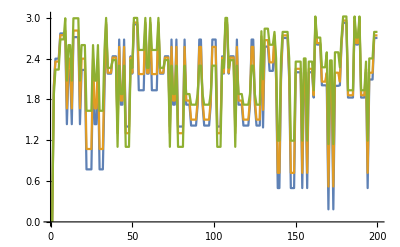

```mathematica
ListLinePlot[Table[rdn[[n]],{n,1,3}]]
```

```mathematica
rdnmax=Table[{0.05*(n-1)*Pi,Max[rdn[[n]]]},{n,1,21}]
```

{{0.,2.92566252216925715},{0.15708,2.95912259826891955},{0.314159,3.01853957553450192},{0.471239,3.12563976364924656},{0.628319,3.15215719644988868},{0.785398,3.02025606035216931},{0.942478,2.7447134102514279},{1.09956,2.37501939704316278},{1.25664,1.96860133334331589},{1.41372,1.67772381211386423},{1.5708,1.57070127429910356},{1.72788,1.67772381211386423},{1.88496,1.96860133334331477},{2.04204,2.37501939704316012},{2.19911,2.74471341025142523},{2.35619,3.02025606035217065},{2.51327,3.15215719644988912},{2.67035,3.12563976364924789},{2.82743,3.01853957553455343},{2.98451,2.95912259826897106},{3.14159,2.92566252216931}}

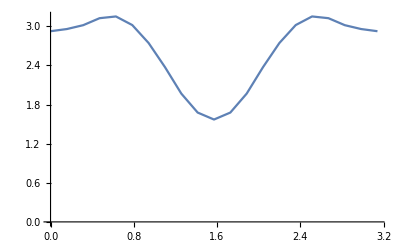

```mathematica
ListLinePlot[rdnmax]
```

```mathematica
rdmean=Table[{0.05 (n-1) Pi,Mean[rdn[[n]]]},{n,1,21}]
```

{{0.,2.00110919332981881},{0.15708,2.06800160133618236},{0.314159,2.18807643082100671},{0.471239,2.27092965495945683},{0.628319,2.25430088160513428},{0.785398,2.11656287828982509},{0.942478,1.87886186434360815},{1.09956,1.58955528931833096},{1.25664,1.31151898104915901},{1.41372,1.10898565474691172},{1.5708,1.03411217379310238},{1.72788,1.10898565474691116},{1.88496,1.31151898104915803},{2.04204,1.58955528931832937},{2.19911,1.87886186434360926},{2.35619,2.11656287828982985},{2.51327,2.25430088160514285},{2.67035,2.27092965495946663},{2.82743,2.18807643082101767},{2.98451,2.06800160133619216},{3.14159,2.00110919332982966}}

#### alt-data

```mathematica
altrd={-0.000000000000000000*10^+00,3.000000000000000000*10^+00,1.653878762572431160*10^+00,1.653878762572431160*10^+00,1.653878762572430938*10^+00,1.565321758921604633*10^+00,1.565321758921604633*10^+00,1.565321758921604633*10^+00,2.426996463741693866*10^+00,7.219778530846886477*10^-01,2.894998244155045697*10^+00,2.894998244155046141*10^+00,7.219778530846903131*10^-01,2.426996463741691201*10^+00,2.426996463741691201*10^+00,2.426996463741691201*10^+00,2.426996463741691201*10^+00,7.219778530846907572*10^-01,2.894998244155040368*10^+00,2.894998244155040812*10^+00,2.894998244155040368*10^+00,2.370609825734585341*10^-01,2.370609825734585341*10^-01,2.370609825734593112*10^-01,2.370609825734592835*10^-01,2.894998244155038591*10^+00,7.219778530846930886*10^-01,7.219778530846938658*10^-01,2.894998244155035927*10^+00,2.370609825734618370*10^-01,2.370609825734616427*10^-01,2.370609825734622256*10^-01,2.456847653392592257*10^+00,2.555975056967317194*10^+00,7.333784714332988175*10^-01,7.333784714332988175*10^-01,7.333784714332991506*10^-01,2.523440563404895975*10^+00,2.523440563404896420*10^+00,2.523440563404895975*10^+00,4.352460909364875286*10^-01,2.888768608110850344*10^+00,1.505513264675413687*10^+00,1.505513264675413687*10^+00,2.888768608110849456*10^+00,4.352460909364886388*10^-01,4.352460909364889163*10^-01,4.352460909364888053*10^-01,2.523440563404892423*10^+00,7.333784714333010379*10^-01,2.555975056967310977*10^+00,2.555975056967310088*10^+00,2.555975056967310088*10^+00,2.456847653392586928*10^+00,2.456847653392586484*10^+00,2.456847653392586484*10^+00,2.456847653392586039*10^+00,2.555975056967308756*10^+00,7.333784714333029253*10^-01,7.333784714333029253*10^-01,2.555975056967308312*10^+00,2.456847653392584707*10^+00,2.456847653392584707*10^+00,2.456847653392584707*10^+00,2.456847653392583819*10^+00,2.555975056967307424*10^+00,7.333784714333049237*10^-01,7.333784714333044796*10^-01,7.333784714333044796*10^-01,2.523440563404886205*10^+00,2.523440563404886205*10^+00,2.523440563404886205*10^+00,4.352460909364948005*10^-01,2.888768608110838798*10^+00,1.505513264675412355*10^+00,1.505513264675412355*10^+00,2.888768608110837466*10^+00,4.352460909364976871*10^-01,4.352460909364977981*10^-01,4.352460909364976871*10^-01,4.352460909364982977*10^-01,2.888768608110833913*10^+00,1.505513264675412355*10^+00,1.505513264675412355*10^+00,1.505513264675412577*10^+00,1.015929733617194408*10^+00,1.015929733617194408*10^+00,1.015929733617194408*10^+00,1.015929733617194630*10^+00,1.505513264675412355*10^+00,2.888768608110829472*10^+00,2.888768608110829472*10^+00,1.505513264675412799*10^+00,1.015929733617194408*10^+00,1.015929733617194408*10^+00,1.015929733617194630*10^+00,1.015929733617195074*10^+00,1.505513264675412577*10^+00,2.888768608110826364*10^+00,2.888768608110825920*10^+00,2.888768608110825920*10^+00,4.352460909365054587*10^-01,4.352460909365060138*10^-01,4.352460909365059583*10^-01,2.523440563404872883*10^+00,7.333784714333100307*10^-01,2.555975056967294101*10^+00,2.555975056967294101*10^+00,7.333784714333119181*10^-01,2.523440563404870218*10^+00,2.523440563404870218*10^+00,2.523440563404870218*10^+00,4.352460909365097330*10^-01,2.888768608110817482*10^+00,1.505513264675411911*10^+00,1.505513264675411689*10^+00,1.505513264675412133*10^+00,1.015929733617197073*10^+00,1.015929733617197295*10^+00,1.015929733617197295*10^+00,1.015929733617197295*10^+00,1.505513264675412577*10^+00,2.888768608110814817*10^+00,2.888768608110813929*10^+00,1.505513264675412355*10^+00,1.015929733617197739*10^+00,1.015929733617197739*10^+00,1.015929733617197961*10^+00,2.906387996381300187*10^+00,5.759458941328647885*10^-01,2.593461078758423355*10^+00,2.593461078758423355*10^+00,2.593461078758422467*10^+00,7.735243727889281606*10^-01,7.735243727889280496*10^-01,7.735243727889283827*10^-01,2.373658940400817485*10^+00,2.760529485966633167*10^+00,4.639597498105275941*10^-02,4.639597498105275941*10^-02,2.760529485966633167*10^+00,2.373658940400815265*10^+00,2.373658940400814377*10^+00,2.373658940400814821*10^+00,2.373658940400814821*10^+00,2.760529485966632279*10^+00,4.639597498105573620*10^-02,4.639597498105573620*10^-02,4.639597498105661744*10^-02,2.923118818799254726*10^+00,2.923118818799254726*10^+00,2.923118818799254282*10^+00,2.923118818799254282*10^+00,4.639597498105880319*10^-02,2.760529485966626950*10^+00,2.760529485966627394*10^+00,4.639597498105951096*10^-02,2.923118818799251617*10^+00,2.923118818799251173*10^+00,2.923118818799250729*10^+00,1.013633817945881699*10^+00,2.316748166957776078*10^+00,1.808548800735001016*10^+00,1.808548800735001016*10^+00,1.808548800735001016*10^+00,1.276161933434055928*10^+00,1.276161933434055928*10^+00,1.276161933434055928*10^+00,2.952987834508085552*10^+00,1.195597622701517586*10^-03,2.930811437051251467*10^+00,2.930811437051251911*10^+00,1.195597622704078038*10^-03,2.952987834508080667*10^+00,2.952987834508079779*10^+00,2.952987834508079779*10^+00,1.276161933434054596*10^+00,1.808548800734998130*10^+00,2.316748166957770749*10^+00,2.316748166957770305*10^+00,2.316748166957770305*10^+00,1.013633817945884363*10^+00,1.013633817945884807*10^+00,1.013633817945885029*10^+00,1.013633817945885029*10^+00,2.316748166957768085*10^+00,1.808548800734996576*10^+00,1.808548800734997020*10^+00,2.316748166957768529*10^+00,1.013633817945884363*10^+00,1.013633817945884363*10^+00,1.013633817945884363*10^+00,2.923118818799234298*10^+00,4.639597498107592144*10^-02,2.760529485966612295*10^+00,2.760529485966612295*10^+00,2.760529485966611851*10^+00,2.373658940400799722*10^+00,2.373658940400799722*10^+00,2.373658940400799278*10^+00,2.722912528242654327*10^-14,2.998724663313188987*10^+00,1.752358915133834349*10^+00,1.752358915133822359*10^+00,1.752358915133833905*10^+00,1.778826252950366893*10^+00,1.778826252950179709*10^+00,1.778826252950367115*10^+00,2.450044033094810114*10^+00,1.004923073174349479*10^+00,2.928752756824851478*10^+00,2.928752756824748893*10^+00,1.004923073174350368*10^+00,2.450044033094807006*10^+00,2.450044033094807450*10^+00,2.450044033094807006*10^+00,2.450044033094807006*10^+00,1.004923073174351256*10^+00,2.928752756824846148*10^+00,2.928752756824743120*10^+00,2.928752756824846593*10^+00,5.756163831610693338*10^-01,5.756163831610692228*10^-01,5.756163831610698889*10^-01,5.756163831610697779*10^-01,2.928752756824740455*10^+00,1.004923073174352810*10^+00,1.004923073174353476*10^+00,2.928752756824842152*10^+00,5.756163831610717763*10^-01,5.756163831610715542*10^-01,5.756163831610719983*10^-01,2.454099128123173656*10^+00,2.619160311581513412*10^+00,9.542317723232556226*10^-01,9.542317723232559556*10^-01,9.542317723232559556*10^-01,2.667908950781288535*10^+00,2.667908950781288091*10^+00,2.667908950781288091*10^+00,4.534545617599395895*10^-01,2.880137060406872340*10^+00,1.590786248270745551*10^+00,1.590786248270745551*10^+00,2.880137060406871896*10^+00,4.534545617599443079*10^-01,4.534545617599419209*10^-01,4.534545617599450296*10^-01,2.667908950781281874*10^+00,9.542317723232577320*10^-01,2.619160311581506750*10^+00,2.619160311581506750*10^+00,2.619160311581506750*10^+00,2.454099128123166995*10^+00,2.454099128123166551*10^+00,2.454099128123166551*10^+00,2.454099128123166551*10^+00,2.619160311581505418*10^+00,9.542317723232592863*10^-01,9.542317723232593973*10^-01,2.619160311581504086*10^+00,2.454099128123164775*10^+00,2.454099128123165219*10^+00,2.454099128123164775*10^+00,2.454099128123164775*10^+00,2.619160311581502754*10^+00,9.542317723232600635*10^-01,9.542317723232598414*10^-01,9.542317723232598414*10^-01,2.667908950781275657*10^+00,2.667908950781275212*10^+00,2.667908950781275212*10^+00,4.534545617599474165*10^-01,2.880137060406859462*10^+00,1.590786248270744441*10^+00,1.590786248270743997*10^+00,2.880137060406859018*10^+00,4.534545617599526901*10^-01,4.534545617599502476*10^-01,4.534545617599527456*10^-01,4.534545617599505807*10^-01,2.880137060406855465*10^+00,1.590786248270743553*10^+00,1.590786248270743553*10^+00,1.590786248270743330*10^+00,1.215424640119457500*10^+00,1.215424640119457056*10^+00,1.215424640119457056*10^+00,1.215424640119457944*10^+00,1.590786248270742664*10^+00,2.880137060406852356*10^+00,2.880137060406851912*10^+00,1.590786248270742220*10^+00,1.215424640119457500*10^+00,1.215424640119457722*10^+00,1.215424640119457278*10^+00,1.215424640119457722*10^+00,1.590786248270742220*10^+00,2.880137060406848359*10^+00,2.880137060406847915*10^+00,2.880137060406847915*10^+00,4.534545617599604617*10^-01,4.534545617599580192*10^-01,4.534545617599607947*10^-01,2.667908950781261446*10^+00,9.542317723232652815*10^-01,2.619160311581487210*10^+00,2.619160311581487210*10^+00,9.542317723232662807*10^-01,2.667908950781257005*10^+00,2.667908950781257893*10^+00,2.667908950781257449*10^+00,4.534545617599627931*10^-01,2.880137060406839034*10^+00,1.590786248270741554*10^+00,1.590786248270741332*10^+00,1.590786248270741332*10^+00,1.215424640119461053*10^+00,1.215424640119460609*10^+00,1.215424640119461275*10^+00,1.215424640119460831*10^+00,1.590786248270741110*10^+00,2.880137060406835037*10^+00,2.880137060406834593*10^+00,1.590786248270741332*10^+00,1.215424640119459720*10^+00,1.215424640119460165*10^+00,1.215424640119460609*10^+00,2.906656314638607963*10^+00,9.361093464075678217*10^-01,2.629146730499057227*10^+00,2.629146730499093199*10^+00,2.629146730499057227*10^+00,1.115180274682690209*10^+00,1.115180274682690209*10^+00,1.115180274682690431*10^+00,2.397117719698572458*10^+00,2.787274539306693555*10^+00,3.046399528917699273*10^-01,3.046399528917700383*10^-01,2.787274539306691779*10^+00,2.397117719698570237*10^+00,2.397117719698570237*10^+00,2.397117719698569793*10^+00,2.397117719698569793*10^+00,2.787274539306690446*10^+00,3.046399528917726474*10^-01,3.046399528917725363*10^-01,3.046399528917730359*10^-01,2.919480822055393165*10^+00,2.919480822055393165*10^+00,2.919480822055393165*10^+00,2.919480822055392721*10^+00,3.046399528917754784*10^-01,2.787274539306685561*10^+00,2.787274539306685561*10^+00,3.046399528917769217*10^-01,2.919480822055388280*10^+00,2.919480822055387836*10^+00,2.919480822055387836*10^+00,1.062158262575489953*10^+00,2.420561697369322918*10^+00,1.875498643463705539*10^+00,1.875498643463705761*10^+00,1.875498643463705761*10^+00,1.466228929068149167*10^+00,1.466228929068149611*10^+00,1.466228929068150055*10^+00,2.951241737549627153*10^+00,4.257787615604939901*10^-01,2.904151562273749931*10^+00,2.904151562272182296*10^+00,4.257787615604948228*10^-01,2.951241737549623601*10^+00,2.951241737549623156*10^+00,2.951241737549623156*10^+00,1.466228929068149167*10^+00,1.875498643463702875*10^+00,2.420561697369317145*10^+00,2.420561697369316700*10^+00,2.420561697369317145*10^+00,1.062158262575495060*10^+00,1.062158262575493728*10^+00,1.062158262575495060*10^+00,1.062158262575493284*10^+00,2.420561697369314480*10^+00,1.875498643463702209*10^+00,1.875498643463702209*10^+00,2.420561697369313592*10^+00,1.062158262575495282*10^+00,1.062158262575493950*10^+00,1.062158262575496392*10^+00,2.919480822055371405*10^+00,3.046399528917894672*10^-01,2.787274539306670018*10^+00,2.787274539306669130*10^+00,2.787274539306669574*10^+00,2.397117719698553362*10^+00,2.397117719698552030*10^+00,2.397117719698552918*10^+00,-9.610279511444755881*10^-16,2.981416978993569611*10^+00,2.032098565832024750*10^+00,2.032098565832025194*10^+00,2.032098565832024750*10^+00,2.253902263947621165*10^+00,2.253902263947621609*10^+00,2.253902263947620721*10^+00,2.616603485375486926*10^+00,1.608797191196068566*10^+00,2.964220781648387870*10^+00,2.964220781648387870*10^+00,1.608797191196069454*10^+00,2.616603485375484262*10^+00,2.616603485375484706*10^+00,2.616603485375484262*10^+00,2.616603485375483373*10^+00,1.608797191196069010*10^+00,2.964220781648383429*10^+00,2.964220781648383429*10^+00,2.964220781648383429*10^+00,1.299572736581438459*10^+00,1.299572736581438015*10^+00,1.299572736581438237*10^+00,1.299572736581437571*10^+00,2.964220781648380321*10^+00,1.608797191196068121*10^+00,1.608797191196069010*10^+00,2.964220781648379432*10^+00,1.299572736581438903*10^+00,1.299572736581438681*10^+00,1.299572736581438681*10^+00,2.494503586821630314*10^+00,2.837513983773300108*10^+00,1.431569600622463634*10^+00,1.431569600622464078*10^+00,1.431569600622464078*10^+00,2.921472429720327835*10^+00,2.921472429720328279*10^+00,2.921472429720326947*10^+00,5.588789635031052860*10^-01,2.855391282629188510*10^+00,1.816817142892695136*10^+00,1.816817142892695802*10^+00,2.855391282629188066*10^+00,5.588789635031078395*10^-01,5.588789635031071734*10^-01,5.588789635031075065*10^-01,2.921472429720321173*10^+00,1.431569600622464078*10^+00,2.837513983773293003*10^+00,2.837513983773291670*10^+00,2.837513983773291670*10^+00,2.494503586821624097*10^+00,2.494503586821623209*10^+00,2.494503586821623209*10^+00,2.494503586821622765*10^+00,2.837513983773290782*10^+00,1.431569600622464966*10^+00,1.431569600622465188*10^+00,2.837513983773289450*10^+00,2.494503586821620988*10^+00,2.494503586821620544*10^+00,2.494503586821620544*10^+00,2.494503586821620544*10^+00,2.837513983773287674*10^+00,1.431569600622465632*10^+00,1.431569600622464966*10^+00,1.431569600622465188*10^+00,2.921472429720313624*10^+00,2.921472429720313624*10^+00,2.921472429720313624*10^+00,5.588789635031136127*10^-01,2.855391282629174743*10^+00,1.816817142892692027*10^+00,1.816817142892692027*10^+00,2.855391282629175187*10^+00,5.588789635031163883*10^-01,5.588789635031161662*10^-01,5.588789635031159442*10^-01,5.588789635031166103*10^-01,2.855391282629170746*10^+00,1.816817142892691361*10^+00,1.816817142892690917*10^+00,1.816817142892691139*10^+00,1.702623940755064513*10^+00,1.702623940755064069*10^+00,1.702623940755063847*10^+00,1.702623940755063847*10^+00,1.816817142892691139*10^+00,2.855391282629167193*10^+00,2.855391282629167637*10^+00,1.816817142892690917*10^+00,1.702623940755062737*10^+00,1.702623940755063181*10^+00,1.702623940755062293*10^+00,1.702623940755062737*10^+00,1.816817142892689141*10^+00,2.855391282629164529*10^+00,2.855391282629163197*10^+00,2.855391282629164529*10^+00,5.588789635031228276*10^-01,5.588789635031223835*10^-01,5.588789635031228276*10^-01,2.921472429720298081*10^+00,1.431569600622462080*10^+00,2.837513983773272130*10^+00,2.837513983773272130*10^+00,1.431569600622463190*10^+00,2.921472429720294972*10^+00,2.921472429720295416*10^+00,2.921472429720294972*10^+00,5.588789635031254921*10^-01,2.855391282629157423*10^+00,1.816817142892688697*10^+00,1.816817142892689141*10^+00,1.816817142892688475*10^+00,1.702623940755061405*10^+00,1.702623940755060961*10^+00,1.702623940755060961*10^+00,1.702623940755060961*10^+00,1.816817142892687809*10^+00,2.855391282629153427*10^+00,2.855391282629152538*10^+00,1.816817142892687365*10^+00,1.702623940755060516*10^+00,1.702623940755060516*10^+00,1.702623940755060961*10^+00,2.990306744670162775*10^+00,1.676550775138237137*10^+00,2.739876671449396284*10^+00,2.739876671449395396*10^+00,2.739876671449396284*10^+00,1.759937298568109210*10^+00,1.759937298568109210*10^+00,1.759937298568109654*10^+00,2.518085677107031906*10^+00,2.940256810949172017*10^+00,8.110111209627411943*10^-01,8.110111209627411943*10^-01,2.940256810949168909*10^+00,2.518085677107030129*10^+00,2.518085677107030129*10^+00,2.518085677107030129*10^+00,2.518085677107029685*10^+00,2.940256810949167576*10^+00,8.110111209627430817*10^-01,8.110111209627430817*10^-01,8.110111209627435258*10^-01,2.953913019438091592*10^+00,2.953913019438091592*10^+00,2.953913019438089815*10^+00,2.953913019438090704*10^+00,8.110111209627446360*10^-01,2.940256810949163135*10^+00,2.940256810949162247*10^+00,8.110111209627464124*10^-01,2.953913019438086263*10^+00,2.953913019438086263*10^+00,2.953913019438086707*10^+00,1.279978255315884716*10^+00,2.692200378572843888*10^+00,2.131309069514921273*10^+00,2.131309069514921717*10^+00,2.131309069514921273*10^+00,1.936977903057280237*10^+00,1.936977903057280237*10^+00,1.936977903057279793*10^+00,2.985717628658073775*10^+00,1.175335481365923584*10^+00,2.892636316284755704*10^+00,2.892636316284755260*10^+00,1.175335481365924473*10^+00,2.985717628658070222*10^+00,2.985717628658068890*10^+00,2.985717628658068890*10^+00,1.936977903057278461*10^+00,2.131309069514918164*10^+00,2.692200378572836783*10^+00,2.692200378572835895*10^+00,2.692200378572835007*10^+00,1.279978255315886493*10^+00,1.279978255315886715*10^+00,1.279978255315886493*10^+00,1.279978255315887159*10^+00,2.692200378572833230*10^+00,2.131309069514916832*10^+00,2.131309069514916388*10^+00,2.692200378572833230*10^+00,1.279978255315886715*10^+00,1.279978255315886937*10^+00,1.279978255315887381*10^+00,2.953913019438069831*10^+00,8.110111209627547391*10^-01,2.940256810949143151*10^+00,2.940256810949142707*10^+00,2.940256810949142707*10^+00,2.518085677107011922*10^+00,2.518085677107011477*10^+00,2.518085677107011477*10^+00,1.121199276335220928*10^-15,2.918699367482326057*10^+00,2.378172886805836939*10^+00,2.378172886805837827*10^+00,2.378172886805837827*10^+00,2.711235124928574436*10^+00,2.711235124928574436*10^+00,2.711235124928573992*10^+00,2.844122254746352496*10^+00,2.149951084200536489*10^+00,2.902223055774761473*10^+00,2.902223055774761029*10^+00,2.149951084200536044*10^+00,2.844122254746349832*10^+00,2.844122254746348943*10^+00,2.844122254746349387*10^+00,2.844122254746349387*10^+00,2.149951084200534268*10^+00,2.902223055774757032*10^+00,2.902223055774756588*10^+00,2.902223055774757032*10^+00,1.950647923353098001*10^+00,1.950647923353098445*10^+00,1.950647923353098223*10^+00,1.950647923353098667*10^+00,2.902223055774754812*10^+00,2.149951084200534268*10^+00,2.149951084200533824*10^+00,2.902223055774752591*10^+00,1.950647923353097779*10^+00,1.950647923353098001*10^+00,1.950647923353097335*10^+00,2.628626434814758106*10^+00,3.078461337815798338*10^+00,1.959766857539623652*10^+00,1.959766857539624096*10^+00,1.959766857539623208*10^+00,3.092458303962505095*10^+00,3.092458303962504651*10^+00,3.092458303962503763*10^+00,7.883573746611693966*10^-01,2.809380203008010390*10^+00,2.179219029580152345*10^+00,2.179219029580152345*10^+00,2.809380203008009058*10^+00,7.883573746611700628*10^-01,7.883573746611701738*10^-01,7.883573746611701738*10^-01,3.092458303962499766*10^+00,1.959766857539620988*10^+00,3.078461337815789456*10^+00,3.078461337815789456*10^+00,3.078461337815789456*10^+00,2.628626434814749224*10^+00,2.628626434814749224*10^+00,2.628626434814749224*10^+00,2.628626434814749668*10^+00,3.078461337815787680*10^+00,1.959766857539619433*10^+00,1.959766857539620322*10^+00,3.078461337815785015*10^+00,2.628626434814747448*10^+00,2.628626434814747448*10^+00,2.628626434814747448*10^+00,2.628626434814747448*10^+00,3.078461337815784127*10^+00,1.959766857539618989*10^+00,1.959766857539618545*10^+00,1.959766857539619433*10^+00,3.092458303962489996*10^+00,3.092458303962489996*10^+00,3.092458303962490884*10^+00,7.883573746611750588*10^-01,2.809380203007998844*10^+00,2.179219029580147016*10^+00,2.179219029580146572*10^+00,2.809380203007997956*10^+00,7.883573746611756139*10^-01,7.883573746611760580*10^-01,7.883573746611762800*10^-01,7.883573746611763911*10^-01,2.809380203007995291*10^+00,2.179219029580144351*10^+00,2.179219029580145239*10^+00,2.179219029580145239*10^+00,2.234856885613236255*10^+00,2.234856885613237143*10^+00,2.234856885613237143*10^+00,2.234856885613236699*10^+00,2.179219029580143463*10^+00,2.809380203007991739*10^+00,2.809380203007991739*10^+00,2.179219029580143463*10^+00,2.234856885613234923*10^+00,2.234856885613234923*10^+00,2.234856885613234923*10^+00,2.234856885613234034*10^+00,2.179219029580142575*10^+00,2.809380203007989518*10^+00,2.809380203007989074*10^+00,2.809380203007988630*10^+00,7.883573746611813871*10^-01,7.883573746611816091*10^-01,7.883573746611820532*10^-01,3.092458303962474453*10^+00,1.959766857539613438*10^+00,3.078461337815764587*10^+00,3.078461337815764587*10^+00,1.959766857539612772*10^+00,3.092458303962472677*10^+00,3.092458303962472677*10^+00,3.092458303962471788*10^+00,7.883573746611831634*10^-01,2.809380203007982413*10^+00,2.179219029580139022*10^+00,2.179219029580139022*10^+00,2.179219029580139910*10^+00,2.234856885613230038*10^+00,2.234856885613230482*10^+00,2.234856885613230926*10^+00,2.234856885613230926*10^+00,2.179219029580139022*10^+00,2.809380203007980192*10^+00,2.809380203007979304*10^+00,2.179219029580139022*10^+00,2.234856885613229149*10^+00,2.234856885613229593*10^+00,2.234856885613229149*10^+00,3.123037102515344277*10^+00,2.358278997438387314*10^+00,2.838627135826218062*10^+00,2.838627135826218950*10^+00,2.838627135826217618*10^+00,2.378902673452628402*10^+00,2.378902673452628402*10^+00,2.378902673452627958*10^+00,2.735666000776487472*10^+00,3.094976227986288908*10^+00,1.392744502347189606*10^+00,1.392744502347189162*10^+00,3.094976227986285799*10^+00,2.735666000776484807*10^+00,2.735666000776485252*10^+00,2.735666000776485696*10^+00,2.735666000776484363*10^+00,3.094976227986284467*10^+00,1.392744502347190050*10^+00,1.392744502347189606*10^+00,1.392744502347190272*10^+00,2.954404042802485364*10^+00,2.954404042802485364*10^+00,2.954404042802484920*10^+00,2.954404042802484476*10^+00,1.392744502347190716*10^+00,3.094976227986280026*10^+00,3.094976227986280026*10^+00,1.392744502347190716*10^+00,2.954404042802480923*10^+00,2.954404042802480479*10^+00,2.954404042802480479*10^+00,1.602045628638260721*10^+00,2.941272221230827544*10^+00,2.484296598450105975*10^+00,2.484296598450105975*10^+00,2.484296598450105087*10^+00,2.434293999192132407*10^+00,2.434293999192131963*10^+00,2.434293999192131963*10^+00,3.015654371386152999*10^+00,1.847866799741942234*10^+00,2.864127170015022372*10^+00,2.864127170015022372*10^+00,1.847866799741942900*10^+00,3.015654371386149002*10^+00,3.015654371386148558*10^+00,3.015654371386149002*10^+00,2.434293999192129299*10^+00,2.484296598450101534*10^+00,2.941272221230819550*10^+00,2.941272221230819106*10^+00,2.941272221230819994*10^+00,1.602045628638260943*10^+00,1.602045628638260943*10^+00,1.602045628638260943*10^+00,1.602045628638261165*10^+00,2.941272221230816442*10^+00,2.484296598450099758*10^+00,2.484296598450099314*10^+00,2.941272221230815997*10^+00,1.602045628638260721*10^+00,1.602045628638260943*10^+00,1.602045628638260943*10^+00,2.954404042802464048*10^+00,1.392744502347193158*10^+00,3.094976227986259598*10^+00,3.094976227986258710*10^+00,3.094976227986259154*10^+00,2.735666000776465712*10^+00,2.735666000776464823*10^+00,2.735666000776466156*10^+00,4.805139755722374982*10^-16,2.787556124351335818*10^+00,2.622903474035252813*10^+00,2.622903474035253701*10^+00,2.622903474035252813*10^+00,2.981903827271191076*10^+00,2.981903827271190632*10^+00,2.981903827271190188*10^+00,3.022253686131202599*10^+00,2.487184057790558622*10^+00,2.714462246835276815*10^+00,2.714462246835276815*10^+00,2.487184057790559955*10^+00,3.022253686131199935*10^+00,3.022253686131199935*10^+00,3.022253686131199935*10^+00,3.022253686131199490*10^+00,2.487184057790557290*10^+00,2.714462246835273262*10^+00,2.714462246835273262*10^+00,2.714462246835273262*10^+00,2.397455296103001565*10^+00,2.397455296103001565*10^+00,2.397455296103000677*10^+00,2.397455296103000677*10^+00,2.714462246835271930*10^+00,2.487184057790555958*10^+00,2.487184057790555958*10^+00,2.714462246835269266*10^+00,2.397455296102999789*10^+00,2.397455296102999345*10^+00,2.397455296102998901*10^+00,2.761138014488604409*10^+00,3.206202020780002826*10^+00,2.351153284384460918*10^+00,2.351153284384460918*10^+00,2.351153284384460473*10^+00,3.008457583852616857*10^+00,3.008457583852616413*10^+00,3.008457583852615969*10^+00,1.021312889350203035*10^+00,2.639929082019596418*10^+00,2.457565383680101245*10^+00,2.457565383680101245*10^+00,2.639929082019595974*10^+00,1.021312889350204367*10^+00,1.021312889350203923*10^+00,1.021312889350204145*10^+00,3.008457583852612416*10^+00,2.351153284384458253*10^+00,3.206202020779993944*10^+00,3.206202020779993056*10^+00,3.206202020779993056*10^+00,2.761138014488597303*10^+00,2.761138014488596859*10^+00,2.761138014488596859*10^+00,2.761138014488595971*10^+00,3.206202020779991280*10^+00,2.351153284384454700*10^+00,2.351153284384455588*10^+00,3.206202020779989503*10^+00,2.761138014488595083*10^+00,2.761138014488594195*10^+00,2.761138014488595083*10^+00,2.761138014488594639*10^+00,3.206202020779987283*10^+00,2.351153284384453812*10^+00,2.351153284384453368*10^+00,2.351153284384452924*10^+00,3.008457583852603090*10^+00,3.008457583852603534*10^+00,3.008457583852603978*10^+00,1.021312889350208586*10^+00,2.639929082019586204*10^+00,2.457565383680093696*10^+00,2.457565383680092364*10^+00,2.639929082019586204*10^+00,1.021312889350209474*10^+00,1.021312889350209030*10^+00,1.021312889350209696*10^+00,1.021312889350209918*10^+00,2.639929082019584872*10^+00,2.457565383680091919*10^+00,2.457565383680091031*10^+00,2.457565383680091031*10^+00,2.629534715346787621*10^+00,2.629534715346788509*10^+00,2.629534715346787177*10^+00,2.629534715346787621*10^+00,2.457565383680089699*10^+00,2.639929082019581763*10^+00,2.639929082019581763*10^+00,2.457565383680088811*10^+00,2.629534715346785401*10^+00,2.629534715346784512*10^+00,2.629534715346785401*10^+00,2.629534715346784512*10^+00,2.457565383680087923*10^+00,2.639929082019578654*10^+00,2.639929082019578654*10^+00,2.639929082019578210*10^+00,1.021312889350213915*10^+00,1.021312889350214137*10^+00,1.021312889350213471*10^+00,3.008457583852588435*10^+00,2.351153284384444042*10^+00,3.206202020779967743*10^+00,3.206202020779966855*10^+00,2.351153284384443154*10^+00,3.008457583852585326*10^+00,3.008457583852585326*10^+00,3.008457583852584882*10^+00,1.021312889350215691*10^+00,2.639929082019571993*10^+00,2.457565383680082149*10^+00,2.457565383680083482*10^+00,2.457565383680082594*10^+00,2.629534715346777407*10^+00,2.629534715346776963*10^+00,2.629534715346777407*10^+00,2.629534715346776963*10^+00,2.457565383680081705*10^+00,2.639929082019570217*10^+00,2.639929082019570661*10^+00,2.457565383680081261*10^+00,2.629534715346774298*10^+00,2.629534715346774298*10^+00,2.629534715346773410*10^+00,3.182309930848526314*10^+00,2.742227077011844649*10^+00,2.836300619422114533*10^+00,2.836300619422115421*10^+00,2.836300619422114533*10^+00,2.797507044208007443*10^+00,2.797507044208007887*10^+00,2.797507044208007443*10^+00,2.918519129504666410*10^+00,3.158339294702029676*10^+00,1.863951032204902880*10^+00,1.863951032204903102*10^+00,3.158339294702027900*10^+00,2.918519129504663301*10^+00,2.918519129504664189*10^+00,2.918519129504663745*10^+00,2.918519129504662857*10^+00,3.158339294702025679*10^+00,1.863951032204903102*10^+00,1.863951032204902880*10^+00,1.863951032204903102*10^+00,2.816659495300577021*10^+00,2.816659495300576577*10^+00,2.816659495300577465*10^+00,2.816659495300576133*10^+00,1.863951032204901992*10^+00,3.158339294702022571*10^+00,3.158339294702022571*10^+00,1.863951032204901548*10^+00,2.816659495300574356*10^+00,2.816659495300573468*10^+00,2.816659495300573468*10^+00,1.887910187454773236*10^+00,3.009826012489591918*10^+00,2.775733365163396638*10^+00,2.775733365163397526*10^+00,2.775733365163396194*10^+00,2.763772287133352101*10^+00,2.763772287133351213*10^+00,2.763772287133351213*10^+00,2.926721688606695793*10^+00,2.235963499210866789*10^+00,2.814350514425385974*10^+00,2.814350514425385974*10^+00,2.235963499210867234*10^+00,2.926721688606693128*10^+00,2.926721688606693128*10^+00,2.926721688606693128*10^+00,2.763772287133347660*10^+00,2.775733365163391753*10^+00,3.009826012489583924*10^+00,3.009826012489583924*10^+00,3.009826012489583924*10^+00,1.887910187454771460*10^+00,1.887910187454771016*10^+00,1.887910187454771016*10^+00,1.887910187454771016*10^+00,3.009826012489581704*10^+00,2.775733365163389976*10^+00,2.775733365163389532*10^+00,3.009826012489579483*10^+00,1.887910187454770128*10^+00,1.887910187454770572*10^+00,1.887910187454770128*10^+00,2.816659495300561478*10^+00,1.863951032204897551*10^+00,3.158339294702002586*10^+00,3.158339294702000810*10^+00,3.158339294702001254*10^+00,2.918519129504643761*10^+00,2.918519129504642429*10^+00,2.918519129504642429*10^+00,3.203426503814917641*10^-16,2.587309775975491721*10^+00,2.693259470988000004*10^+00,2.693259470988000448*10^+00,2.693259470987999116*10^+00,3.011307784282112543*10^+00,3.011307784282111655*10^+00,3.011307784282110767*10^+00,3.045941629743476486*10^+00,2.522895322711246280*10^+00,2.408589727685536808*10^+00,2.408589727685536808*10^+00,2.522895322711244948*10^+00,3.045941629743472934*10^+00,3.045941629743472490*10^+00,3.045941629743472490*10^+00,3.045941629743471601*10^+00,2.522895322711244503*10^+00,2.408589727685535919*10^+00,2.408589727685535919*10^+00,2.408589727685535031*10^+00,2.544291272193394349*10^+00,2.544291272193394349*10^+00,2.544291272193393905*10^+00,2.544291272193394349*10^+00,2.408589727685535031*10^+00,2.522895322711241839*10^+00,2.522895322711240951*10^+00,2.408589727685533255*10^+00,2.544291272193391684*10^+00,2.544291272193392128*10^+00,2.544291272193392128*10^+00,2.819707802335920110*10^+00,3.143499705688424406*10^+00,2.525826712364926507*10^+00,2.525826712364927396*10^+00,2.525826712364926507*10^+00,2.626497258940618362*10^+00,2.626497258940618806*10^+00,2.626497258940617474*10^+00,1.143242573435591769*10^+00,2.431978856870995465*10^+00,2.574541377158669597*10^+00,2.574541377158670041*10^+00,2.431978856870994576*10^+00,1.143242573435592657*10^+00,1.143242573435592435*10^+00,1.143242573435592657*10^+00,2.626497258940616142*10^+00,2.525826712364922511*10^+00,3.143499705688415968*10^+00,3.143499705688415080*10^+00,3.143499705688414636*10^+00,2.819707802335911673*10^+00,2.819707802335911229*10^+00,2.819707802335911229*10^+00,2.819707802335910785*10^+00,3.143499705688412860*10^+00,2.525826712364920290*10^+00,2.525826712364920290*10^+00,3.143499705688411083*10^+00,2.819707802335909452*10^+00,2.819707802335909008*10^+00,2.819707802335909008*10^+00,2.819707802335909452*10^+00,3.143499705688409307*10^+00,2.525826712364918514*10^+00,2.525826712364918070*10^+00,2.525826712364918070*10^+00,2.626497258940610813*10^+00,2.626497258940610369*10^+00,2.626497258940610369*10^+00,1.143242573435596654*10^+00,2.431978856870987915*10^+00,2.574541377158662492*10^+00,2.574541377158661604*10^+00,2.431978856870987471*10^+00,1.143242573435597320*10^+00,1.143242573435597320*10^+00,1.143242573435597320*10^+00,1.143242573435597764*10^+00,2.431978856870986583*10^+00,2.574541377158660271*10^+00,2.574541377158658939*10^+00,2.574541377158658939*10^+00,2.840354282011927634*10^+00,2.840354282011927634*10^+00,2.840354282011927634*10^+00,2.840354282011928078*10^+00,2.574541377158657607*10^+00,2.431978856870983918*10^+00,2.431978856870984362*10^+00,2.574541377158657607*10^+00,2.840354282011924525*10^+00,2.840354282011925413*10^+00,2.840354282011924525*10^+00,2.840354282011925413*10^+00,2.574541377158656275*10^+00,2.431978856870982586*10^+00,2.431978856870982586*10^+00,2.431978856870982142*10^+00,1.143242573435600651*10^+00,1.143242573435600207*10^+00,1.143242573435600651*10^+00,2.626497258940601931*10^+00,2.525826712364906967*10^+00,3.143499705688392432*10^+00,3.143499705688391099*10^+00,2.525826712364906079*10^+00,2.626497258940600155*10^+00,2.626497258940599711*10^+00,2.626497258940598378*10^+00,1.143242573435602871*10^+00,2.431978856870978145*10^+00,2.574541377158650945*10^+00,2.574541377158651834*10^+00,2.574541377158650945*10^+00,2.840354282011915199*10^+00,2.840354282011914755*10^+00,2.840354282011914755*10^+00,2.840354282011914755*10^+00,2.574541377158650057*10^+00,2.431978856870976813*10^+00,2.431978856870976369*10^+00,2.574541377158649169*10^+00,2.840354282011912535*10^+00,2.840354282011912090*10^+00,2.840354282011912090*10^+00,3.113598287612116877*10^+00,2.789030180280604565*10^+00,2.694520141118066814*10^+00,2.694520141118065482*10^+00,2.694520141118065482*10^+00,2.961864201206129366*10^+00,2.961864201206130254*10^+00,2.961864201206128921*10^+00,2.995503486097826240*10^+00,3.057066242724542526*10^+00,2.091151977914319282*10^+00,2.091151977914319726*10^+00,3.057066242724541638*10^+00,2.995503486097824020*10^+00,2.995503486097822687*10^+00,2.995503486097823131*10^+00,2.995503486097822243*10^+00,3.057066242724540306*10^+00,2.091151977914317062*10^+00,2.091151977914317506*10^+00,2.091151977914317950*10^+00,2.448844877347862603*10^+00,2.448844877347862603*10^+00,2.448844877347863047*10^+00,2.448844877347862603*10^+00,2.091151977914317506*10^+00,3.057066242724535865*10^+00,3.057066242724536309*10^+00,2.091151977914317506*10^+00,2.448844877347860827*10^+00,2.448844877347861271*10^+00,2.448844877347860827*10^+00,1.965654414691549112*10^+00,2.917240837199871706*10^+00,2.912385498755017288*10^+00,2.912385498755018176*10^+00,2.912385498755017288*10^+00,2.889370923872210284*10^+00,2.889370923872210284*10^+00,2.889370923872209396*10^+00,2.727056540969713616*10^+00,2.308149107461414218*10^+00,2.710041993571228325*10^+00,2.710041993571228325*10^+00,2.308149107461413774*10^+00,2.727056540969710952*10^+00,2.727056540969711396*10^+00,2.727056540969710952*10^+00,2.889370923872205843*10^+00,2.912385498755012403*10^+00,2.917240837199865933*10^+00,2.917240837199865933*10^+00,2.917240837199865044*10^+00,1.965654414691548002*10^+00,1.965654414691547336*10^+00,1.965654414691546892*10^+00,1.965654414691546670*10^+00,2.917240837199862824*10^+00,2.912385498755008850*10^+00,2.912385498755009294*10^+00,2.917240837199861936*10^+00,1.965654414691547558*10^+00,1.965654414691546670*10^+00,1.965654414691546892*10^+00,2.448844877347851945*10^+00,2.091151977914311288*10^+00,3.057066242724518101*10^+00,3.057066242724517213*10^+00,3.057066242724517657*10^+00,2.995503486097801815*10^+00,2.995503486097800927*10^+00,2.995503486097801371*10^+00,-9.610279511444755881*10^-16,2.341986164786201030*10^+00,2.551145534378439717*10^+00,2.551145534378439717*10^+00,2.551145534378439272*10^+00,2.841890338961801987*10^+00,2.841890338961802431*10^+00,2.841890338961802875*10^+00,2.883712111054717919*10^+00,2.378111612160871413*10^+00,2.078379611164755225*10^+00,2.078379611164756113*10^+00,2.378111612160870525*10^+00,2.883712111054715699*10^+00,2.883712111054714367*10^+00,2.883712111054713922*10^+00,2.883712111054713478*10^+00,2.378111612160869637*10^+00,2.078379611164754337*10^+00,2.078379611164753449*10^+00,2.078379611164753449*10^+00,2.458933106327104046*10^+00,2.458933106327103602*10^+00,2.458933106327103157*10^+00,2.458933106327102713*10^+00,2.078379611164753449*10^+00,2.378111612160868304*10^+00,2.378111612160868304*10^+00,2.078379611164753005*10^+00,2.458933106327100937*10^+00,2.458933106327100937*10^+00,2.458933106327100049*10^+00,2.734188962403508505*10^+00,2.874636414331015022*10^+00,2.452694213623218822*10^+00,2.452694213623217934*10^+00,2.452694213623217934*10^+00,2.039104369570182040*10^+00,2.039104369570182484*10^+00,2.039104369570182484*10^+00,1.094462279687554718*10^+00,2.237248941914798284*10^+00,2.498548003508126669*10^+00,2.498548003508126669*10^+00,2.237248941914797395*10^+00,1.094462279687556050*10^+00,1.094462279687556494*10^+00,1.094462279687556272*10^+00,2.039104369570182484*10^+00,2.452694213623215713*10^+00,2.874636414331010137*10^+00,2.874636414331009249*10^+00,2.874636414331009249*10^+00,2.734188962403502288*10^+00,2.734188962403500955*10^+00,2.734188962403500067*10^+00,2.734188962403500511*10^+00,2.874636414331007472*10^+00,2.452694213623212605*10^+00,2.452694213623212605*10^+00,2.874636414331007028*10^+00,2.734188962403500511*10^+00,2.734188962403498735*10^+00,2.734188962403499179*10^+00,2.734188962403498291*10^+00,2.874636414331005252*10^+00,2.452694213623211716*10^+00,2.452694213623211716*10^+00,2.452694213623211716*10^+00,2.039104369570181152*10^+00,2.039104369570180708*10^+00,2.039104369570180708*10^+00,1.094462279687561601*10^+00,2.237248941914791622*10^+00,2.498548003508120008*10^+00,2.498548003508120008*10^+00,2.237248941914791178*10^+00,1.094462279687563377*10^+00,1.094462279687563155*10^+00,1.094462279687563377*10^+00,1.094462279687562933*10^+00,2.237248941914789846*10^+00,2.498548003508116899*10^+00,2.498548003508117787*10^+00,2.498548003508116899*10^+00,2.791426019912747414*10^+00,2.791426019912746526*10^+00,2.791426019912745193*10^+00,2.791426019912745637*10^+00,2.498548003508116899*10^+00,2.237248941914788958*10^+00,2.237248941914788958*10^+00,2.498548003508116011*10^+00,2.791426019912743861*10^+00,2.791426019912742973*10^+00,2.791426019912742973*10^+00,2.791426019912742085*10^+00,2.498548003508115123*10^+00,2.237248941914787626*10^+00,2.237248941914787626*10^+00,2.237248941914787181*10^+00,1.094462279687568040*10^+00,1.094462279687567818*10^+00,1.094462279687567374*10^+00,2.039104369570178932*10^+00,2.452694213623201502*10^+00,2.874636414330990597*10^+00,2.874636414330989709*10^+00,2.452694213623200170*10^+00,2.039104369570178488*10^+00,2.039104369570178044*10^+00,2.039104369570178488*10^+00,1.094462279687570039*10^+00,2.237248941914783629*10^+00,2.498548003508110238*10^+00,2.498548003508109794*10^+00,2.498548003508109794*10^+00,2.791426019912734091*10^+00,2.791426019912733203*10^+00,2.791426019912734091*10^+00,2.791426019912732759*10^+00,2.498548003508108906*10^+00,2.237248941914782296*10^+00,2.237248941914782296*10^+00,2.498548003508108017*10^+00,2.791426019912731427*10^+00,2.791426019912731427*10^+00,2.791426019912731427*10^+00,2.908879474821532085*10^+00,2.580892302182117515*10^+00,2.435689648537634255*10^+00,2.435689648537634255*10^+00,2.435689648537633367*10^+00,2.888338183384265623*10^+00,2.888338183384264291*10^+00,2.888338183384264735*10^+00,2.906392579421159361*10^+00,2.758748655027598140*10^+00,2.091815090440047875*10^+00,2.091815090440047431*10^+00,2.758748655027598140*10^+00,2.906392579421157585*10^+00,2.906392579421157585*10^+00,2.906392579421156697*10^+00,2.906392579421156697*10^+00,2.758748655027596808*10^+00,2.091815090440046987*10^+00,2.091815090440046099*10^+00,2.091815090440046543*10^+00,1.949786540628495324*10^+00,1.949786540628493992*10^+00,1.949786540628494436*10^+00,1.949786540628494880*10^+00,2.091815090440046543*10^+00,2.758748655027593255*10^+00,2.758748655027593255*10^+00,2.091815090440045211*10^+00,1.949786540628494214*10^+00,1.949786540628494436*10^+00,1.949786540628493547*10^+00,1.814947413271316590*10^+00,2.720961858943349299*10^+00,2.814458561271660830*10^+00,2.814458561271660386*10^+00,2.814458561271660386*10^+00,2.822361512837658015*10^+00,2.822361512837657571*10^+00,2.822361512837657571*10^+00,2.449770528255895030*10^+00,2.142941437694469986*10^+00,2.516795523896746989*10^+00,2.516795523896746101*10^+00,2.142941437694468654*10^+00,2.449770528255893254*10^+00,2.449770528255893254*10^+00,2.449770528255893254*10^+00,2.822361512837653574*10^+00,2.814458561271656389*10^+00,2.720961858943343081*10^+00,2.720961858943343525*10^+00,2.720961858943342637*10^+00,1.814947413271316590*10^+00,1.814947413271316590*10^+00,1.814947413271316368*10^+00,1.814947413271316590*10^+00,2.720961858943341305*10^+00,2.814458561271652393*10^+00,2.814458561271652393*10^+00,2.720961858943339973*10^+00,1.814947413271316812*10^+00,1.814947413271316590*10^+00,1.814947413271315702*10^+00,1.949786540628491327*10^+00,2.091815090440038993*10^+00,2.758748655027579488*10^+00,2.758748655027578600*10^+00,2.758748655027579488*10^+00,2.906392579421138045*10^+00,2.906392579421135824*10^+00,2.906392579421137157*10^+00,-3.203426503814917641*10^-16,2.091405684522766428*10^+00,2.238344451623535569*10^+00,2.238344451623535125*10^+00,2.238344451623535125*10^+00,2.513493380930929888*10^+00,2.513493380930930332*10^+00,2.513493380930930332*10^+00,2.563625601356354977*10^+00,2.129560884721700909*10^+00,1.797586180292075841*10^+00,1.797586180292075841*10^+00,2.129560884721700909*10^+00,2.563625601356352757*10^+00,2.563625601356353201*10^+00,2.563625601356352757*10^+00,2.563625601356352757*10^+00,2.129560884721700464*10^+00,1.797586180292075397*10^+00,1.797586180292075175*10^+00,1.797586180292075841*10^+00,2.218310302478091245*10^+00,2.218310302478091245*10^+00,2.218310302478090801*10^+00,2.218310302478090357*10^+00,1.797586180292074953*10^+00,2.129560884721700020*10^+00,2.129560884721700020*10^+00,1.797586180292074953*10^+00,2.218310302478089469*10^+00,2.218310302478089469*10^+00,2.218310302478089469*10^+00,2.500098281458440486*10^+00,2.453810217124395177*10^+00,2.228629444809790972*10^+00,2.228629444809790972*10^+00,2.228629444809790527*10^+00,1.423552763088210993*10^+00,1.423552763088212325*10^+00,1.423552763088213213*10^+00,9.325011323333831648*10^-01,2.067514786875571886*10^+00,2.236433488289675253*10^+00,2.236433488289675253*10^+00,2.067514786875571886*10^+00,9.325011323333863844*10^-01,9.325011323333860513*10^-01,9.325011323333859403*10^-01,1.423552763088216322*10^+00,2.228629444809787863*10^+00,2.453810217124392068*10^+00,2.453810217124391180*10^+00,2.453810217124391180*10^+00,2.500098281458436045*10^+00,2.500098281458434712*10^+00,2.500098281458435601*10^+00,2.500098281458435157*10^+00,2.453810217124390292*10^+00,2.228629444809787419*10^+00,2.228629444809786975*10^+00,2.453810217124389403*10^+00,2.500098281458432936*10^+00,2.500098281458433824*10^+00,2.500098281458432936*10^+00,2.500098281458433380*10^+00,2.453810217124389403*10^+00,2.228629444809785642*10^+00,2.228629444809786975*10^+00,2.228629444809786087*10^+00,1.423552763088218764*10^+00,1.423552763088215878*10^+00,1.423552763088220097*10^+00,9.325011323333929347*10^-01,2.067514786875567889*10^+00,2.236433488289670812*10^+00,2.236433488289669924*10^+00,2.067514786875568333*10^+00,9.325011323333958213*10^-01,9.325011323333953772*10^-01,9.325011323333952662*10^-01,9.325011323333955993*10^-01,2.067514786875567445*10^+00,2.236433488289669924*10^+00,2.236433488289669924*10^+00,2.236433488289670368*10^+00,2.541359346173948097*10^+00,2.541359346173949429*10^+00,2.541359346173948097*10^+00,2.541359346173948541*10^+00,2.236433488289669036*10^+00,2.067514786875567001*10^+00,2.067514786875566113*10^+00,2.236433488289669036*10^+00,2.541359346173946321*10^+00,2.541359346173947209*10^+00,2.541359346173945877*10^+00,2.541359346173946321*10^+00,2.236433488289667704*10^+00,2.067514786875566113*10^+00,2.067514786875565225*10^+00,2.067514786875566113*10^+00,9.325011323334018165*10^-01,9.325011323334011504*10^-01,9.325011323334012614*10^-01,1.423552763088223871*10^+00,2.228629444809779869*10^+00,2.453810217124379633*10^+00,2.453810217124379633*10^+00,2.228629444809777649*10^+00,1.423552763088222983*10^+00,1.423552763088224760*10^+00,1.423552763088224760*10^+00,9.325011323334045921*10^-01,2.067514786875563892*10^+00,2.236433488289665483*10^+00,2.236433488289664595*10^+00,2.236433488289664595*10^+00,2.541359346173938771*10^+00,2.541359346173939660*10^+00,2.541359346173938327*10^+00,2.541359346173937883*10^+00,2.236433488289664151*10^+00,2.067514786875563004*10^+00,2.067514786875563892*10^+00,2.236433488289665039*10^+00,2.541359346173936995*10^+00,2.541359346173935663*10^+00,2.541359346173935663*10^+00,2.599507659039236529*10^+00,2.242548586515508813*10^+00,2.079429426472815923*10^+00,2.079429426472815923*10^+00,2.079429426472815035*10^+00,2.634022906109458440*10^+00,2.634022906109459328*10^+00,2.634022906109458884*10^+00,2.653668864069258504*10^+00,2.321661115564246369*10^+00,1.927263414842319111*10^+00,1.927263414842319111*10^+00,2.321661115564246369*10^+00,2.653668864069258504*10^+00,2.653668864069257616*10^+00,2.653668864069257172*10^+00,2.653668864069257616*10^+00,2.321661115564245481*10^+00,1.927263414842317779*10^+00,1.927263414842317779*10^+00,1.927263414842317557*10^+00,1.481979738582924977*10^+00,1.481979738582924533*10^+00,1.481979738582924755*10^+00,1.481979738582924977*10^+00,1.927263414842317779*10^+00,2.321661115564242817*10^+00,2.321661115564242372*10^+00,1.927263414842318001*10^+00,1.481979738582925643*10^+00,1.481979738582924755*10^+00,1.481979738582925421*10^+00,1.528925304291061993*10^+00,2.472311172015396963*10^+00,2.509200410430720840*10^+00,2.509200410430720396*10^+00,2.509200410430720840*10^+00,2.570847725945612616*10^+00,2.570847725945613504*10^+00,2.570847725945613504*10^+00,2.172076028496858768*10^+00,1.851223791392154761*10^+00,2.240873503122491783*10^+00,2.240873503122491783*10^+00,1.851223791392155427*10^+00,2.172076028496857436*10^+00,2.172076028496856992*10^+00,2.172076028496857436*10^+00,2.570847725945610840*10^+00,2.509200410430717731*10^+00,2.472311172015393410*10^+00,2.472311172015392078*10^+00,2.472311172015392966*10^+00,1.528925304291065768*10^+00,1.528925304291065101*10^+00,1.528925304291064879*10^+00,1.528925304291065324*10^+00,2.472311172015391190*10^+00,2.509200410430715955*10^+00,2.509200410430715955*10^+00,2.472311172015390746*10^+00,1.528925304291066212*10^+00,1.528925304291066212*10^+00,1.528925304291066434*10^+00,1.481979738582930528*10^+00,1.927263414842313116*10^+00,2.321661115564236155*10^+00,2.321661115564237043*10^+00,2.321661115564236155*10^+00,2.653668864069242073*10^+00,2.653668864069241184*10^+00,2.653668864069242073*10^+00,-3.203426503814917641*10^-16,1.877982233341431550*10^+00,1.882588405754049843*10^+00,1.882588405754049843*10^+00,1.882588405754049399*10^+00,2.118068242758665232*10^+00,2.118068242758665676*10^+00,2.118068242758664788*10^+00,2.215321868563694618*10^+00,1.837707686528976758*10^+00,1.603190888440548356*10^+00,1.603190888440549022*10^+00,1.837707686528976758*10^+00,2.215321868563694174*10^+00,2.215321868563694174*10^+00,2.215321868563693730*10^+00,2.215321868563693286*10^+00,1.837707686528977202*10^+00,1.603190888440549466*10^+00,1.603190888440549688*10^+00,1.603190888440549244*10^+00,1.912513198383415602*10^+00,1.912513198383414492*10^+00,1.912513198383414936*10^+00,1.912513198383415380*10^+00,1.603190888440550133*10^+00,1.837707686528976758*10^+00,1.837707686528976536*10^+00,1.603190888440550799*10^+00,1.912513198383413604*10^+00,1.912513198383414492*10^+00,1.912513198383414048*10^+00,2.166504498997806394*10^+00,2.019003493536946081*10^+00,1.954999068588024747*10^+00,1.954999068588024302*10^+00,1.954999068588024747*10^+00,9.592423783605565912*10^-01,9.592423783605567023*10^-01,9.592423783605575904*10^-01,7.384072550297149373*10^-01,1.912617497182143911*10^+00,1.874015016119793264*10^+00,1.874015016119793264*10^+00,1.912617497182144133*10^+00,7.384072550297172688*10^-01,7.384072550297179349*10^-01,7.384072550297180459*10^-01,9.592423783605611431*10^-01,1.954999068588023192*10^+00,2.019003493536945193*10^+00,2.019003493536945193*10^+00,2.019003493536945193*10^+00,2.166504498997803729*10^+00,2.166504498997803729*10^+00,2.166504498997803285*10^+00,2.166504498997803285*10^+00,2.019003493536945193*10^+00,1.954999068588023192*10^+00,1.954999068588023414*10^+00,2.019003493536945193*10^+00,2.166504498997802841*10^+00,2.166504498997803285*10^+00,2.166504498997802841*10^+00,2.166504498997802841*10^+00,2.019003493536945193*10^+00,1.954999068588022970*10^+00,1.954999068588023192*10^+00,1.954999068588022970*10^+00,9.592423783605686927*10^-01,9.592423783605686927*10^-01,9.592423783605685816*10^-01,7.384072550297287041*10^-01,1.912617497182141912*10^+00,1.874015016119793042*10^+00,1.874015016119792820*10^+00,1.912617497182142579*10^+00,7.384072550297307025*10^-01,7.384072550297305915*10^-01,7.384072550297308135*10^-01,7.384072550297311466*10^-01,1.912617497182141690*10^+00,1.874015016119792820*10^+00,1.874015016119793486*10^+00,1.874015016119793486*10^+00,2.184860454483435799*10^+00,2.184860454483435355*10^+00,2.184860454483435799*10^+00,2.184860454483435355*10^+00,1.874015016119793930*10^+00,1.912617497182142134*10^+00,1.912617497182142134*10^+00,1.874015016119793486*10^+00,2.184860454483434022*10^+00,2.184860454483434022*10^+00,2.184860454483434022*10^+00,2.184860454483433578*10^+00,1.874015016119794153*10^+00,1.912617497182142134*10^+00,1.912617497182142579*10^+00,1.912617497182141912*10^+00,7.384072550297400284*10^-01,7.384072550297392512*10^-01,7.384072550297398063*10^-01,9.592423783605805720*10^-01,1.954999068588020306*10^+00,2.019003493536941196*10^+00,2.019003493536941196*10^+00,1.954999068588019417*10^+00,9.592423783605822374*10^-01,9.592423783605820153*10^-01,9.592423783605814602*10^-01,7.384072550297441362*10^-01,1.912617497182139914*10^+00,1.874015016119792820*10^+00,1.874015016119792598*10^+00,1.874015016119793264*10^+00,2.184860454483429582*10^+00,2.184860454483429582*10^+00,2.184860454483429582*10^+00,2.184860454483430470*10^+00,1.874015016119793042*10^+00,1.912617497182140580*10^+00,1.912617497182140136*10^+00,1.874015016119793042*10^+00,2.184860454483428693*10^+00,2.184860454483428693*10^+00,2.184860454483428693*10^+00,2.288386226928134981*10^+00,1.879373861374439958*10^+00,1.757209429011760804*10^+00,1.757209429011761248*10^+00,1.757209429011761026*10^+00,2.296442906428138642*10^+00,2.296442906428139086*10^+00,2.296442906428137753*10^+00,2.311147526972417765*10^+00,1.863434681090834433*10^+00,1.690953481855435703*10^+00,1.690953481855435925*10^+00,1.863434681090834877*10^+00,2.311147526972417321*10^+00,2.311147526972417765*10^+00,2.311147526972416877*10^+00,2.311147526972417321*10^+00,1.863434681090834433*10^+00,1.690953481855435259*10^+00,1.690953481855435259*10^+00,1.690953481855436591*10^+00,1.168707530282446561*10^+00,1.168707530282446783*10^+00,1.168707530282447005*10^+00,1.168707530282446783*10^+00,1.690953481855435925*10^+00,1.863434681090834211*10^+00,1.863434681090833767*10^+00,1.690953481855436147*10^+00,1.168707530282448337*10^+00,1.168707530282449003*10^+00,1.168707530282447671*10^+00,1.259681092018989146*10^+00,2.215824090647169342*10^+00,2.088126599539872785*10^+00,2.088126599539872785*10^+00,2.088126599539873229*10^+00,2.231085507359238385*10^+00,2.231085507359237496*10^+00,2.231085507359237496*10^+00,1.913785636838553295*10^+00,1.511312688172453012*10^+00,1.934826296600093976*10^+00,1.934826296600093531*10^+00,1.511312688172453678*10^+00,1.913785636838553073*10^+00,1.913785636838553739*10^+00,1.913785636838552850*10^+00,2.231085507359236164*10^+00,2.088126599539872341*10^+00,2.215824090647167122*10^+00,2.215824090647166678*10^+00,2.215824090647167566*10^+00,1.259681092018995141*10^+00,1.259681092018995141*10^+00,1.259681092018994697*10^+00,1.259681092018993587*10^+00,2.215824090647166678*10^+00,2.088126599539871009*10^+00,2.088126599539871009*10^+00,2.215824090647165789*10^+00,1.259681092018996473*10^+00,1.259681092018997361*10^+00,1.259681092018996695*10^+00,1.168707530282457885*10^+00,1.690953481855436147*10^+00,1.863434681090834211*10^+00,1.863434681090834655*10^+00,1.863434681090834655*10^+00,2.311147526972408439*10^+00,2.311147526972407551*10^+00,2.311147526972407995*10^+00,-6.406853007629837254*10^-16,1.735984017267223400*10^+00,1.585388507147007520*10^+00,1.585388507147006631*10^+00,1.585388507147006187*10^+00,1.799654850193672662*10^+00,1.799654850193672218*10^+00,1.799654850193671773*10^+00,1.920236269785954519*10^+00,1.591664867768447289*10^+00,1.432408743514639538*10^+00,1.432408743514640204*10^+00,1.591664867768448399*10^+00,1.920236269785954963*10^+00,1.920236269785954519*10^+00,1.920236269785954741*10^+00,1.920236269785954519*10^+00,1.591664867768449731*10^+00,1.432408743514640426*10^+00,1.432408743514641314*10^+00,1.432408743514641314*10^+00,1.650996719282789016*10^+00,1.650996719282787684*10^+00,1.650996719282788128*10^+00,1.650996719282787684*10^+00,1.432408743514641980*10^+00,1.591664867768450176*10^+00,1.591664867768449287*10^+00,1.432408743514642202*10^+00,1.650996719282788350*10^+00,1.650996719282787684*10^+00,1.650996719282788128*10^+00,1.906652996944802947*10^+00,1.657624551424333736*10^+00,1.731905401730330141*10^+00,1.731905401730328808*10^+00,1.731905401730329030*10^+00,6.758770293092801751*10^-01,6.758770293092801751*10^-01,6.758770293092803971*10^-01,6.419985061189859010*10^-01,1.779196727053080185*10^+00,1.549401040404532193*10^+00,1.549401040404531527*10^+00,1.779196727053080185*10^+00,6.419985061189891207*10^-01,6.419985061189892317*10^-01,6.419985061189893427*10^-01,6.758770293092855042*10^-01,1.731905401730328808*10^+00,1.657624551424335291*10^+00,1.657624551424335291*10^+00,1.657624551424335291*10^+00,1.906652996944802503*10^+00,1.906652996944802281*10^+00,1.906652996944802503*10^+00,1.906652996944801615*10^+00,1.657624551424336179*10^+00,1.731905401730329697*10^+00,1.731905401730329475*10^+00,1.657624551424336179*10^+00,1.906652996944802281*10^+00,1.906652996944802281*10^+00,1.906652996944802947*10^+00,1.906652996944801837*10^+00,1.657624551424336179*10^+00,1.731905401730330807*10^+00,1.731905401730331029*10^+00,1.731905401730330363*10^+00,6.758770293092947190*10^-01,6.758770293092946080*10^-01,6.758770293092959403*10^-01,6.419985061190017772*10^-01,1.779196727053079741*10^+00,1.549401040404535301*10^+00,1.549401040404535745*10^+00,1.779196727053080851*10^+00,6.419985061190056630*10^-01,6.419985061190057740*10^-01,6.419985061190046638*10^-01,6.419985061190062181*10^-01,1.779196727053079741*10^+00,1.549401040404537300*10^+00,1.549401040404536412*10^+00,1.549401040404536634*10^+00,1.868029679175142066*10^+00,1.868029679175142288*10^+00,1.868029679175141400*10^+00,1.868029679175141400*10^+00,1.549401040404537522*10^+00,1.779196727053079963*10^+00,1.779196727053080629*10^+00,1.549401040404537966*10^+00,1.868029679175140956*10^+00,1.868029679175141844*10^+00,1.868029679175141844*10^+00,1.868029679175141622*10^+00,1.549401040404537744*10^+00,1.779196727053080407*10^+00,1.779196727053081073*10^+00,1.779196727053080407*10^+00,6.419985061190139897*10^-01,6.419985061190146558*10^-01,6.419985061190145448*10^-01,6.758770293093103732*10^-01,1.731905401730330363*10^+00,1.657624551424338621*10^+00,1.657624551424337955*10^+00,1.731905401730330141*10^+00,6.758770293093130377*10^-01,6.758770293093127046*10^-01,6.758770293093137038*10^-01,6.419985061190208731*10^-01,1.779196727053080185*10^+00,1.549401040404540630*10^+00,1.549401040404540630*10^+00,1.549401040404540408*10^+00,1.868029679175140512*10^+00,1.868029679175140734*10^+00,1.868029679175140956*10^+00,1.868029679175139846*10^+00,1.549401040404541074*10^+00,1.779196727053080185*10^+00,1.779196727053079741*10^+00,1.549401040404541297*10^+00,1.868029679175140290*10^+00,1.868029679175140068*10^+00,1.868029679175140068*10^+00,2.046098090587788576*10^+00,1.587550380743742329*10^+00,1.535516067690767095*10^+00,1.535516067690766873*10^+00,1.535516067690766873*10^+00,2.000475437959671865*10^+00,2.000475437959671865*10^+00,2.000475437959671421*10^+00,2.033716050980518553*10^+00,1.485499518421384169*10^+00,1.481884321224694379*10^+00,1.481884321224693712*10^+00,1.485499518421383947*10^+00,2.033716050980518109*10^+00,2.033716050980518553*10^+00,2.033716050980518109*10^+00,2.033716050980517664*10^+00,1.485499518421384835*10^+00,1.481884321224694823*10^+00,1.481884321224694601*10^+00,1.481884321224695267*10^+00,1.035253754961509509*10^+00,1.035253754961509065*10^+00,1.035253754961510175*10^+00,1.035253754961509509*10^+00,1.481884321224694823*10^+00,1.485499518421385279*10^+00,1.485499518421385279*10^+00,1.481884321224695711*10^+00,1.035253754961510175*10^+00,1.035253754961510619*10^+00,1.035253754961510841*10^+00,1.053017726174441560*10^+00,2.012588570155026346*10^+00,1.725332204936325553*10^+00,1.725332204936326885*10^+00,1.725332204936325331*10^+00,1.932026921545858311*10^+00,1.932026921545858089*10^+00,1.932026921545857867*10^+00,1.711147755613698695*10^+00,1.275412661822644900*10^+00,1.684554093855737289*10^+00,1.684554093855736845*10^+00,1.275412661822645344*10^+00,1.711147755613698251*10^+00,1.711147755613698918*10^+00,1.711147755613698473*10^+00,1.932026921545857423*10^+00,1.725332204936325997*10^+00,2.012588570155024570*10^+00,2.012588570155023682*10^+00,2.012588570155023682*10^+00,1.053017726174449109*10^+00,1.053017726174449109*10^+00,1.053017726174449109*10^+00,1.053017726174449553*10^+00,2.012588570155023238*10^+00,1.725332204936326441*10^+00,1.725332204936326885*10^+00,2.012588570155022794*10^+00,1.053017726174451774*10^+00,1.053017726174451330*10^+00,1.053017726174451107*10^+00,1.035253754961523498*10^+00,1.481884321224698819*10^+00,1.485499518421390830*10^+00,1.485499518421390830*10^+00,1.485499518421390608*10^+00,2.033716050980513224*10^+00,2.033716050980513224*10^+00,2.033716050980513224*10^+00,-0.000000000000000000*10^+00,1.686361081672271389*10^+00,1.447833566860163401*10^+00,1.447833566860162957*10^+00,1.447833566860162957*10^+00,1.673919939337090046*10^+00,1.673919939337089158*10^+00,1.673919939337089602*10^+00,1.812461946684777780*10^+00,1.493314689661152439*10^+00,1.355779597875445663*10^+00,1.355779597875445219*10^+00,1.493314689661153327*10^+00,1.812461946684776670*10^+00,1.812461946684776670*10^+00,1.812461946684777114*10^+00,1.812461946684776892*10^+00,1.493314689661153771*10^+00,1.355779597875446774*10^+00,1.355779597875446330*10^+00,1.355779597875446107*10^+00,1.546229168966754219*10^+00,1.546229168966753775*10^+00,1.546229168966753775*10^+00,1.546229168966754219*10^+00,1.355779597875447884*10^+00,1.493314689661153327*10^+00,1.493314689661154659*10^+00,1.355779597875448106*10^+00,1.546229168966753997*10^+00,1.546229168966753775*10^+00,1.546229168966753775*10^+00,1.802626488011647377*10^+00,1.506757637872679467*10^+00,1.626465844897910351*10^+00,1.626465844897908575*10^+00,1.626465844897909463*10^+00,6.122851032677371075*10^-01,6.122851032677377736*10^-01,6.122851032677377736*10^-01,5.919229329218100855*10^-01,1.734565426989859827*10^+00,1.416210582899800841*10^+00,1.416210582899800396*10^+00,1.734565426989861825*10^+00,5.919229329218126390*10^-01,5.919229329218127500*10^-01,5.919229329218123059*10^-01,6.122851032677443239*10^-01,1.626465844897909463*10^+00,1.506757637872680800*10^+00,1.506757637872679911*10^+00,1.506757637872679911*10^+00,1.802626488011647155*10^+00,1.802626488011645600*10^+00,1.802626488011646266*10^+00,1.802626488011646044*10^+00,1.506757637872679911*10^+00,1.626465844897910351*10^+00,1.626465844897909463*10^+00,1.506757637872680800*10^+00,1.802626488011646488*10^+00,1.802626488011645378*10^+00,1.802626488011645822*10^+00,1.802626488011645822*10^+00,1.506757637872681244*10^+00,1.626465844897911239*10^+00,1.626465844897909685*10^+00,1.626465844897910129*10^+00,6.122851032677527616*10^-01,6.122851032677537608*10^-01,6.122851032677527616*10^-01,5.919229329218256286*10^-01,1.734565426989858938*10^+00,1.416210582899803727*10^+00,1.416210582899803283*10^+00,1.734565426989859604*10^+00,5.919229329218291813*10^-01,5.919229329218292923*10^-01,5.919229329218300695*10^-01,5.919229329218295144*10^-01,1.734565426989859160*10^+00,1.416210582899804393*10^+00,1.416210582899804615*10^+00,1.416210582899805281*10^+00,1.750312413680926049*10^+00,1.750312413680925605*10^+00,1.750312413680925161*10^+00,1.750312413680925161*10^+00,1.416210582899805281*10^+00,1.734565426989860271*10^+00,1.734565426989859160*10^+00,1.416210582899805059*10^+00,1.750312413680925383*10^+00,1.750312413680925605*10^+00,1.750312413680924717*10^+00,1.750312413680924939*10^+00,1.416210582899805948*10^+00,1.734565426989859382*10^+00,1.734565426989858494*10^+00,1.734565426989858494*10^+00,5.919229329218388402*10^-01,5.919229329218389513*10^-01,5.919229329218386182*10^-01,6.122851032677699701*10^-01,1.626465844897910795*10^+00,1.506757637872684130*10^+00,1.506757637872683464*10^+00,1.626465844897911239*10^+00,6.122851032677717464*10^-01,6.122851032677720795*10^-01,6.122851032677721905*10^-01,5.919229329218446134*10^-01,1.734565426989856940*10^+00,1.416210582899809056*10^+00,1.416210582899807946*10^+00,1.416210582899807946*10^+00,1.750312413680924939*10^+00,1.750312413680923829*10^+00,1.750312413680923829*10^+00,1.750312413680924051*10^+00,1.416210582899809278*10^+00,1.734565426989858494*10^+00,1.734565426989857162*10^+00,1.416210582899808390*10^+00,1.750312413680924717*10^+00,1.750312413680925383*10^+00,1.750312413680923829*10^+00,1.950860484832435571*10^+00,1.454701798377292077*10^+00,1.437470944739434042*10^+00,1.437470944739433820*10^+00,1.437470944739433820*10^+00,1.888446128944137214*10^+00,1.888446128944137214*10^+00,1.888446128944137214*10^+00,1.925671161492608752*10^+00,1.342458095014931407*10^+00,1.405068967921085266*10^+00,1.405068967921083711*10^+00,1.342458095014931851*10^+00,1.925671161492607641*10^+00,1.925671161492607419*10^+00,1.925671161492607197*10^+00,1.925671161492606753*10^+00,1.342458095014932962*10^+00,1.405068967921085044*10^+00,1.405068967921085044*10^+00,1.405068967921084822*10^+00,1.004081104279225478*10^+00,1.004081104279225034*10^+00,1.004081104279225922*10^+00,1.004081104279225922*10^+00,1.405068967921085710*10^+00,1.342458095014934294*10^+00,1.342458095014933184*10^+00,1.405068967921086820*10^+00,1.004081104279227699*10^+00,1.004081104279227699*10^+00,1.004081104279228365*10^+00,9.772540830382144827*10^-01,1.933399033720421878*10^+00,1.567325714193751773*10^+00,1.567325714193751995*10^+00,1.567325714193751551*10^+00,1.811189379872430560*10^+00,1.811189379872430782*10^+00,1.811189379872430338*10^+00,1.638216730281258471*10^+00,1.177597045189507252*10^+00,1.585728994726429253*10^+00,1.585728994726429253*10^+00,1.177597045189508584*10^+00,1.638216730281258471*10^+00,1.638216730281258249*10^+00,1.638216730281257805*10^+00,1.811189379872429006*10^+00,1.567325714193752217*10^+00,1.933399033720421212*10^+00,1.933399033720419880*10^+00,1.933399033720420324*10^+00,9.772540830382218102*10^-01,9.772540830382232535*10^-01,9.772540830382224764*10^-01,9.772540830382225874*10^-01,1.933399033720419213*10^+00,1.567325714193752884*10^+00,1.567325714193753106*10^+00,1.933399033720419435*10^+00,9.772540830382246968*10^-01,9.772540830382251409*10^-01,9.772540830382243637*10^-01,1.004081104279240133*10^+00,1.405068967921088596*10^+00,1.342458095014939401*10^+00,1.342458095014939623*10^+00,1.342458095014938513*10^+00,1.925671161492603201*10^+00,1.925671161492602090*10^+00,1.925671161492602312*10^+00,-3.203426503814917641*10^-16,1.735984017267223845*10^+00,1.585388507147006854*10^+00,1.585388507147006631*10^+00,1.585388507147006854*10^+00,1.799654850193672218*10^+00,1.799654850193672218*10^+00,1.799654850193672440*10^+00,1.920236269785954519*10^+00,1.591664867768448399*10^+00,1.432408743514640204*10^+00,1.432408743514639982*10^+00,1.591664867768449065*10^+00,1.920236269785954297*10^+00,1.920236269785954075*10^+00,1.920236269785954075*10^+00,1.920236269785953631*10^+00,1.591664867768450176*10^+00,1.432408743514640870*10^+00,1.432408743514641092*10^+00,1.432408743514640870*10^+00,1.650996719282788128*10^+00,1.650996719282787906*10^+00,1.650996719282787684*10^+00,1.650996719282787906*10^+00,1.432408743514642424*10^+00,1.591664867768450620*10^+00,1.591664867768450176*10^+00,1.432408743514642202*10^+00,1.650996719282787684*10^+00,1.650996719282787684*10^+00,1.650996719282788128*10^+00,1.906652996944802947*10^+00,1.657624551424332626*10^+00,1.731905401730328586*10^+00,1.731905401730328808*10^+00,1.731905401730328808*10^+00,6.758770293092815074*10^-01,6.758770293092810633*10^-01,6.758770293092806192*10^-01,6.419985061189860120*10^-01,1.779196727053081073*10^+00,1.549401040404531082*10^+00,1.549401040404530860*10^+00,1.779196727053080851*10^+00,6.419985061189890097*10^-01,6.419985061189892317*10^-01,6.419985061189884545*10^-01,6.758770293092868364*10^-01,1.731905401730329697*10^+00,1.657624551424334403*10^+00,1.657624551424333958*10^+00,1.657624551424333958*10^+00,1.906652996944802947*10^+00,1.906652996944801837*10^+00,1.906652996944802503*10^+00,1.906652996944802059*10^+00,1.657624551424335513*10^+00,1.731905401730329697*10^+00,1.731905401730329475*10^+00,1.657624551424334625*10^+00,1.906652996944802059*10^+00,1.906652996944802059*10^+00,1.906652996944802503*10^+00,1.906652996944802059*10^+00,1.657624551424335735*10^+00,1.731905401730329919*10^+00,1.731905401730330585*10^+00,1.731905401730329697*10^+00,6.758770293092953851*10^-01,6.758770293092960513*10^-01,6.758770293092950521*10^-01,6.419985061190015552*10^-01,1.779196727053080851*10^+00,1.549401040404534857*10^+00,1.549401040404535301*10^+00,1.779196727053080851*10^+00,6.419985061190049969*10^-01,6.419985061190044418*10^-01,6.419985061190052189*10^-01,6.419985061190055520*10^-01,1.779196727053081073*10^+00,1.549401040404535967*10^+00,1.549401040404535967*10^+00,1.549401040404536189*10^+00,1.868029679175140956*10^+00,1.868029679175140956*10^+00,1.868029679175141400*10^+00,1.868029679175142066*10^+00,1.549401040404537078*10^+00,1.779196727053081517*10^+00,1.779196727053080851*10^+00,1.549401040404536634*10^+00,1.868029679175142066*10^+00,1.868029679175141178*10^+00,1.868029679175141622*10^+00,1.868029679175141178*10^+00,1.549401040404537966*10^+00,1.779196727053082183*10^+00,1.779196727053081961*10^+00,1.779196727053082183*10^+00,6.419985061190143227*10^-01,6.419985061190143227*10^-01,6.419985061190138786*10^-01,6.758770293093101511*10^-01,1.731905401730329697*10^+00,1.657624551424336845*10^+00,1.657624551424336401*10^+00,1.731905401730329697*10^+00,6.758770293093132597*10^-01,6.758770293093132597*10^-01,6.758770293093137038*10^-01,6.419985061190198739*10^-01,1.779196727053080629*10^+00,1.549401040404539742*10^+00,1.549401040404540186*10^+00,1.549401040404539964*10^+00,1.868029679175139623*10^+00,1.868029679175140068*10^+00,1.868029679175139623*10^+00,1.868029679175140068*10^+00,1.549401040404540186*10^+00,1.779196727053080851*10^+00,1.779196727053080851*10^+00,1.549401040404541297*10^+00,1.868029679175139623*10^+00,1.868029679175139623*10^+00,1.868029679175139623*10^+00,2.046098090587789464*10^+00,1.587550380743742773*10^+00,1.535516067690767095*10^+00,1.535516067690767539*10^+00,1.535516067690766429*10^+00,2.000475437959670977*10^+00,2.000475437959670977*10^+00,2.000475437959670533*10^+00,2.033716050980517664*10^+00,1.485499518421379950*10^+00,1.481884321224693046*10^+00,1.481884321224692824*10^+00,1.485499518421379506*10^+00,2.033716050980518553*10^+00,2.033716050980517220*10^+00,2.033716050980517664*10^+00,2.033716050980517220*10^+00,1.485499518421380616*10^+00,1.481884321224693046*10^+00,1.481884321224693268*10^+00,1.481884321224693046*10^+00,1.035253754961511063*10^+00,1.035253754961511508*10^+00,1.035253754961511730*10^+00,1.035253754961511286*10^+00,1.481884321224693268*10^+00,1.485499518421381504*10^+00,1.485499518421380838*10^+00,1.481884321224693490*10^+00,1.035253754961513062*10^+00,1.035253754961513284*10^+00,1.035253754961513506*10^+00,1.053017726174441115*10^+00,2.012588570155025902*10^+00,1.725332204936323555*10^+00,1.725332204936323555*10^+00,1.725332204936323777*10^+00,1.932026921545856979*10^+00,1.932026921545856535*10^+00,1.932026921545856535*10^+00,1.711147755613696253*10^+00,1.275412661822642457*10^+00,1.684554093855736845*10^+00,1.684554093855737511*10^+00,1.275412661822643567*10^+00,1.711147755613695587*10^+00,1.711147755613695365*10^+00,1.711147755613695587*10^+00,1.932026921545855869*10^+00,1.725332204936323777*10^+00,2.012588570155024126*10^+00,2.012588570155024570*10^+00,2.012588570155024570*10^+00,1.053017726174449331*10^+00,1.053017726174449331*10^+00,1.053017726174448887*10^+00,1.053017726174449109*10^+00,2.012588570155024126*10^+00,1.725332204936324665*10^+00,1.725332204936324665*10^+00,2.012588570155023682*10^+00,1.053017726174451107*10^+00,1.053017726174452218*10^+00,1.053017726174451996*10^+00,1.035253754961527051*10^+00,1.481884321224696377*10^+00,1.485499518421386611*10^+00,1.485499518421386611*10^+00,1.485499518421387943*10^+00,2.033716050980513668*10^+00,2.033716050980513224*10^+00,2.033716050980513668*10^+00,1.281370601525966465*10^-15,1.877982233341430662*10^+00,1.882588405754048511*10^+00,1.882588405754048066*10^+00,1.882588405754048733*10^+00,2.118068242758663899*10^+00,2.118068242758663899*10^+00,2.118068242758663455*10^+00,2.215321868563693286*10^+00,1.837707686528975426*10^+00,1.603190888440549244*10^+00,1.603190888440548800*10^+00,1.837707686528975426*10^+00,2.215321868563691954*10^+00,2.215321868563692398*10^+00,2.215321868563692398*10^+00,2.215321868563691954*10^+00,1.837707686528975870*10^+00,1.603190888440549910*10^+00,1.603190888440549244*10^+00,1.603190888440549022*10^+00,1.912513198383412938*10^+00,1.912513198383413382*10^+00,1.912513198383413160*10^+00,1.912513198383413160*10^+00,1.603190888440548800*10^+00,1.837707686528975648*10^+00,1.837707686528975648*10^+00,1.603190888440549688*10^+00,1.912513198383413160*10^+00,1.912513198383412272*10^+00,1.912513198383412050*10^+00,2.166504498997805062*10^+00,2.019003493536944305*10^+00,1.954999068588024524*10^+00,1.954999068588024302*10^+00,1.954999068588023636*10^+00,9.592423783605574794*10^-01,9.592423783605562582*10^-01,9.592423783605571463*10^-01,7.384072550297144932*10^-01,1.912617497182143245*10^+00,1.874015016119790600*10^+00,1.874015016119790600*10^+00,1.912617497182143467*10^+00,7.384072550297176019*10^-01,7.384072550297173798*10^-01,7.384072550297174908*10^-01,9.592423783605614762*10^-01,1.954999068588021860*10^+00,2.019003493536943417*10^+00,2.019003493536942972*10^+00,2.019003493536942528*10^+00,2.166504498997802841*10^+00,2.166504498997801509*10^+00,2.166504498997801509*10^+00,2.166504498997801065*10^+00,2.019003493536942528*10^+00,1.954999068588021638*10^+00,1.954999068588022082*10^+00,2.019003493536942528*10^+00,2.166504498997801065*10^+00,2.166504498997801065*10^+00,2.166504498997801065*10^+00,2.166504498997800621*10^+00,2.019003493536943417*10^+00,1.954999068588022304*10^+00,1.954999068588021860*10^+00,1.954999068588021860*10^+00,9.592423783605694698*10^-01,9.592423783605681376*10^-01,9.592423783605698029*10^-01,7.384072550297270388*10^-01,1.912617497182142134*10^+00,1.874015016119790378*10^+00,1.874015016119790822*10^+00,1.912617497182142134*10^+00,7.384072550297292592*10^-01,7.384072550297293702*10^-01,7.384072550297298143*10^-01,7.384072550297297033*10^-01,1.912617497182143023*10^+00,1.874015016119791710*10^+00,1.874015016119791266*10^+00,1.874015016119791266*10^+00,2.184860454483434467*10^+00,2.184860454483434022*10^+00,2.184860454483434467*10^+00,2.184860454483434911*10^+00,1.874015016119791488*10^+00,1.912617497182142134*10^+00,1.912617497182142801*10^+00,1.874015016119791266*10^+00,2.184860454483433578*10^+00,2.184860454483433134*10^+00,2.184860454483433134*10^+00,2.184860454483432690*10^+00,1.874015016119791266*10^+00,1.912617497182142134*10^+00,1.912617497182143023*10^+00,1.912617497182142579*10^+00,7.384072550297384741*10^-01,7.384072550297388071*10^-01,7.384072550297383630*10^-01,9.592423783605813492*10^-01,1.954999068588018751*10^+00,2.019003493536940308*10^+00,2.019003493536939864*10^+00,1.954999068588019195*10^+00,9.592423783605833476*10^-01,9.592423783605821264*10^-01,9.592423783605834586*10^-01,7.384072550297435811*10^-01,1.912617497182142356*10^+00,1.874015016119790822*10^+00,1.874015016119791488*10^+00,1.874015016119791266*10^+00,2.184860454483428693*10^+00,2.184860454483428693*10^+00,2.184860454483427805*10^+00,2.184860454483429137*10^+00,1.874015016119790822*10^+00,1.912617497182141246*10^+00,1.912617497182140358*10^+00,1.874015016119791044*10^+00,2.184860454483427805*10^+00,2.184860454483428249*10^+00,2.184860454483427805*10^+00,2.288386226928134981*10^+00,1.879373861374439292*10^+00,1.757209429011760804*10^+00,1.757209429011761248*10^+00,1.757209429011761248*10^+00,2.296442906428137753*10^+00,2.296442906428137753*10^+00,2.296442906428137309*10^+00,2.311147526972417321*10^+00,1.863434681090830436*10^+00,1.690953481855434593*10^+00,1.690953481855434815*10^+00,1.863434681090831546*10^+00,2.311147526972415989*10^+00,2.311147526972415989*10^+00,2.311147526972416433*10^+00,2.311147526972415545*10^+00,1.863434681090830658*10^+00,1.690953481855436813*10^+00,1.690953481855434370*10^+00,1.690953481855435925*10^+00,1.168707530282450113*10^+00,1.168707530282450335*10^+00,1.168707530282450335*10^+00,1.168707530282450335*10^+00,1.690953481855434593*10^+00,1.863434681090830214*10^+00,1.863434681090830214*10^+00,1.690953481855434593*10^+00,1.168707530282452334*10^+00,1.168707530282452112*10^+00,1.168707530282452556*10^+00,1.259681092018987369*10^+00,2.215824090647170230*10^+00,2.088126599539869677*10^+00,2.088126599539869233*10^+00,2.088126599539869233*10^+00,2.231085507359236608*10^+00,2.231085507359236608*10^+00,2.231085507359235720*10^+00,1.913785636838549298*10^+00,1.511312688172448793*10^+00,1.934826296600094642*10^+00,1.934826296600094642*10^+00,1.511312688172449015*10^+00,1.913785636838548188*10^+00,1.913785636838547966*10^+00,1.913785636838547521*10^+00,2.231085507359233500*10^+00,2.088126599539867900*10^+00,2.215824090647166678*10^+00,2.215824090647166678*10^+00,2.215824090647166678*10^+00,1.259681092018994919*10^+00,1.259681092018994253*10^+00,1.259681092018994475*10^+00,1.259681092018994031*10^+00,2.215824090647167566*10^+00,2.088126599539867012*10^+00,2.088126599539867456*10^+00,2.215824090647166233*10^+00,1.259681092018996029*10^+00,1.259681092018996473*10^+00,1.259681092018996029*10^+00,1.168707530282463214*10^+00,1.690953481855434148*10^+00,1.863434681090829548*10^+00,1.863434681090829770*10^+00,1.863434681090829770*10^+00,2.311147526972406219*10^+00,2.311147526972406663*10^+00,2.311147526972406663*10^+00,1.601713251907458574*10^-16,2.091405684522765096*10^+00,2.238344451623533349*10^+00,2.238344451623533793*10^+00,2.238344451623534237*10^+00,2.513493380930929000*10^+00,2.513493380930929000*10^+00,2.513493380930928556*10^+00,2.563625601356352313*10^+00,2.129560884721699576*10^+00,1.797586180292073843*10^+00,1.797586180292073621*10^+00,2.129560884721698688*10^+00,2.563625601356351424*10^+00,2.563625601356350536*10^+00,2.563625601356350536*10^+00,2.563625601356350536*10^+00,2.129560884721699132*10^+00,1.797586180292074065*10^+00,1.797586180292073621*10^+00,1.797586180292073621*10^+00,2.218310302478088136*10^+00,2.218310302478089024*10^+00,2.218310302478087692*10^+00,2.218310302478088580*10^+00,1.797586180292073399*10^+00,2.129560884721697800*10^+00,2.129560884721697800*10^+00,1.797586180292073621*10^+00,2.218310302478087692*10^+00,2.218310302478086804*10^+00,2.218310302478086804*10^+00,2.500098281458437821*10^+00,2.453810217124390736*10^+00,2.228629444809788307*10^+00,2.228629444809788751*10^+00,2.228629444809788307*10^+00,1.423552763088210549*10^+00,1.423552763088210549*10^+00,1.423552763088209883*10^+00,9.325011323333819435*10^-01,2.067514786875571442*10^+00,2.236433488289670812*10^+00,2.236433488289670812*10^+00,2.067514786875570998*10^+00,9.325011323333846081*10^-01,9.325011323333843860*10^-01,9.325011323333839419*10^-01,1.423552763088212769*10^+00,2.228629444809786087*10^+00,2.453810217124387183*10^+00,2.453810217124386739*10^+00,2.453810217124386295*10^+00,2.500098281458432936*10^+00,2.500098281458432048*10^+00,2.500098281458432048*10^+00,2.500098281458432048*10^+00,2.453810217124385851*10^+00,2.228629444809783866*10^+00,2.228629444809784310*10^+00,2.453810217124385851*10^+00,2.500098281458430716*10^+00,2.500098281458430272*10^+00,2.500098281458431160*10^+00,2.500098281458429827*10^+00,2.453810217124384074*10^+00,2.228629444809783866*10^+00,2.228629444809783422*10^+00,2.228629444809782978*10^+00,1.423552763088218320*10^+00,1.423552763088217654*10^+00,1.423552763088216544*10^+00,9.325011323333908253*10^-01,2.067514786875566557*10^+00,2.236433488289667260*10^+00,2.236433488289666371*10^+00,2.067514786875567445*10^+00,9.325011323333936009*10^-01,9.325011323333938229*10^-01,9.325011323333938229*10^-01,9.325011323333936009*10^-01,2.067514786875567445*10^+00,2.236433488289666371*10^+00,2.236433488289666371*10^+00,2.236433488289666371*10^+00,2.541359346173945877*10^+00,2.541359346173945433*10^+00,2.541359346173945877*10^+00,2.541359346173945877*10^+00,2.236433488289666371*10^+00,2.067514786875565669*10^+00,2.067514786875566557*10^+00,2.236433488289665039*10^+00,2.541359346173943212*10^+00,2.541359346173943212*10^+00,2.541359346173942768*10^+00,2.541359346173943212*10^+00,2.236433488289664595*10^+00,2.067514786875566557*10^+00,2.067514786875565669*10^+00,2.067514786875566113*10^+00,9.325011323333998181*10^-01,9.325011323333993740*10^-01,9.325011323333994850*10^-01,1.423552763088224316*10^+00,2.228629444809776317*10^+00,2.453810217124375637*10^+00,2.453810217124376081*10^+00,2.228629444809776317*10^+00,1.423552763088224982*10^+00,1.423552763088225426*10^+00,1.423552763088224982*10^+00,9.325011323334022606*10^-01,2.067514786875563892*10^+00,2.236433488289661931*10^+00,2.236433488289661042*10^+00,2.236433488289661931*10^+00,2.541359346173936551*10^+00,2.541359346173936107*10^+00,2.541359346173934775*10^+00,2.541359346173935663*10^+00,2.236433488289661042*10^+00,2.067514786875563004*10^+00,2.067514786875562560*10^+00,2.236433488289660154*10^+00,2.541359346173932998*10^+00,2.541359346173934330*10^+00,2.541359346173933886*10^+00,2.599507659039235641*10^+00,2.242548586515505260*10^+00,2.079429426472815479*10^+00,2.079429426472815479*10^+00,2.079429426472815479*10^+00,2.634022906109453555*10^+00,2.634022906109453110*10^+00,2.634022906109453110*10^+00,2.653668864069254507*10^+00,2.321661115564239708*10^+00,1.927263414842315781*10^+00,1.927263414842316225*10^+00,2.321661115564238820*10^+00,2.653668864069252731*10^+00,2.653668864069252287*10^+00,2.653668864069252287*10^+00,2.653668864069251843*10^+00,2.321661115564238376*10^+00,1.927263414842315559*10^+00,1.927263414842316225*10^+00,1.927263414842315559*10^+00,1.481979738582930306*10^+00,1.481979738582928974*10^+00,1.481979738582929862*10^+00,1.481979738582929640*10^+00,1.927263414842314448*10^+00,2.321661115564236155*10^+00,2.321661115564236599*10^+00,1.927263414842314004*10^+00,1.481979738582931860*10^+00,1.481979738582930084*10^+00,1.481979738582930084*10^+00,1.528925304291058440*10^+00,2.472311172015397851*10^+00,2.509200410430716399*10^+00,2.509200410430715955*10^+00,2.509200410430715955*10^+00,2.570847725945609064*10^+00,2.570847725945609064*10^+00,2.570847725945609508*10^+00,2.172076028496852551*10^+00,1.851223791392149209*10^+00,2.240873503122494448*10^+00,2.240873503122494004*10^+00,1.851223791392148099*10^+00,2.172076028496851219*10^+00,2.172076028496850775*10^+00,2.172076028496851219*10^+00,2.570847725945606399*10^+00,2.509200410430711958*10^+00,2.472311172015394298*10^+00,2.472311172015393410*10^+00,2.472311172015393410*10^+00,1.528925304291061327*10^+00,1.528925304291062215*10^+00,1.528925304291061327*10^+00,1.528925304291062215*10^+00,2.472311172015392966*10^+00,2.509200410430711514*10^+00,2.509200410430711514*10^+00,2.472311172015391190*10^+00,1.528925304291062437*10^+00,1.528925304291062659*10^+00,1.528925304291062437*10^+00,1.481979738582936745*10^+00,1.927263414842310674*10^+00,2.321661115564229938*10^+00,2.321661115564229050*10^+00,2.321661115564229050*10^+00,2.653668864069237632*10^+00,2.653668864069236744*10^+00,2.653668864069236744*10^+00,1.441541926716712396*10^-15,2.341986164786199698*10^+00,2.551145534378437052*10^+00,2.551145534378436608*10^+00,2.551145534378436608*10^+00,2.841890338961799767*10^+00,2.841890338961799767*10^+00,2.841890338961799323*10^+00,2.883712111054714811*10^+00,2.378111612160869193*10^+00,2.078379611164755225*10^+00,2.078379611164755225*10^+00,2.378111612160869193*10^+00,2.883712111054712590*10^+00,2.883712111054712146*10^+00,2.883712111054712590*10^+00,2.883712111054712146*10^+00,2.378111612160868304*10^+00,2.078379611164754337*10^+00,2.078379611164754781*10^+00,2.078379611164754337*10^+00,2.458933106327101825*10^+00,2.458933106327100493*10^+00,2.458933106327100937*10^+00,2.458933106327100937*10^+00,2.078379611164753449*10^+00,2.378111612160865640*10^+00,2.378111612160865640*10^+00,2.078379611164753893*10^+00,2.458933106327099605*10^+00,2.458933106327099161*10^+00,2.458933106327099161*10^+00,2.734188962403507173*10^+00,2.874636414331013690*10^+00,2.452694213623217045*10^+00,2.452694213623217045*10^+00,2.452694213623216601*10^+00,2.039104369570182484*10^+00,2.039104369570181596*10^+00,2.039104369570182040*10^+00,1.094462279687554940*10^+00,2.237248941914797840*10^+00,2.498548003508124449*10^+00,2.498548003508124005*10^+00,2.237248941914797395*10^+00,1.094462279687555828*10^+00,1.094462279687555828*10^+00,1.094462279687555828*10^+00,2.039104369570182484*10^+00,2.452694213623213493*10^+00,2.874636414331007472*10^+00,2.874636414331008361*10^+00,2.874636414331008361*10^+00,2.734188962403500511*10^+00,2.734188962403500067*10^+00,2.734188962403500511*10^+00,2.734188962403499623*10^+00,2.874636414331005696*10^+00,2.452694213623211272*10^+00,2.452694213623210828*10^+00,2.874636414331005252*10^+00,2.734188962403496959*10^+00,2.734188962403498291*10^+00,2.734188962403498291*10^+00,2.734188962403496959*10^+00,2.874636414331003476*10^+00,2.452694213623209052*10^+00,2.452694213623208608*10^+00,2.452694213623209496*10^+00,2.039104369570183373*10^+00,2.039104369570182484*10^+00,2.039104369570181596*10^+00,1.094462279687560269*10^+00,2.237248941914792066*10^+00,2.498548003508117343*10^+00,2.498548003508117343*10^+00,2.237248941914792955*10^+00,1.094462279687562045*10^+00,1.094462279687561379*10^+00,1.094462279687561601*10^+00,1.094462279687561157*10^+00,2.237248941914792066*10^+00,2.498548003508116011*10^+00,2.498548003508115567*10^+00,2.498548003508115123*10^+00,2.791426019912744749*10^+00,2.791426019912744749*10^+00,2.791426019912743861*10^+00,2.791426019912744749*10^+00,2.498548003508115567*10^+00,2.237248941914791178*10^+00,2.237248941914791178*10^+00,2.498548003508114235*10^+00,2.791426019912742085*10^+00,2.791426019912741197*10^+00,2.791426019912741197*10^+00,2.791426019912741641*10^+00,2.498548003508113791*10^+00,2.237248941914790290*10^+00,2.237248941914790290*10^+00,2.237248941914790290*10^+00,1.094462279687566042*10^+00,1.094462279687565154*10^+00,1.094462279687565154*10^+00,2.039104369570182929*10^+00,2.452694213623200170*10^+00,2.874636414330989709*10^+00,2.874636414330989709*10^+00,2.452694213623198838*10^+00,2.039104369570184261*10^+00,2.039104369570183817*10^+00,2.039104369570183373*10^+00,1.094462279687566708*10^+00,2.237248941914787626*10^+00,2.498548003508108906*10^+00,2.498548003508108906*10^+00,2.498548003508108017*10^+00,2.791426019912732759*10^+00,2.791426019912732759*10^+00,2.791426019912732315*10^+00,2.791426019912732759*10^+00,2.498548003508108462*10^+00,2.237248941914786293*10^+00,2.237248941914785849*10^+00,2.498548003508106685*10^+00,2.791426019912730094*10^+00,2.791426019912730538*10^+00,2.791426019912730538*10^+00,2.908879474821536526*10^+00,2.580892302182116183*10^+00,2.435689648537637808*10^+00,2.435689648537638252*10^+00,2.435689648537637808*10^+00,2.888338183384264291*10^+00,2.888338183384263402*10^+00,2.888338183384262958*10^+00,2.906392579421157585*10^+00,2.758748655027598140*10^+00,2.091815090440045655*10^+00,2.091815090440046099*10^+00,2.758748655027596808*10^+00,2.906392579421155808*10^+00,2.906392579421154920*10^+00,2.906392579421154920*10^+00,2.906392579421154920*10^+00,2.758748655027596364*10^+00,2.091815090440043878*10^+00,2.091815090440043878*10^+00,2.091815090440043878*10^+00,1.949786540628507536*10^+00,1.949786540628506870*10^+00,1.949786540628505538*10^+00,1.949786540628506648*10^+00,2.091815090440042990*10^+00,2.758748655027593699*10^+00,2.758748655027593255*10^+00,2.091815090440042546*10^+00,1.949786540628506870*10^+00,1.949786540628506426*10^+00,1.949786540628507092*10^+00,1.814947413271316368*10^+00,2.720961858943354628*10^+00,2.814458561271660386*10^+00,2.814458561271660386*10^+00,2.814458561271659498*10^+00,2.822361512837658015*10^+00,2.822361512837656683*10^+00,2.822361512837658459*10^+00,2.449770528255896362*10^+00,2.142941437694466433*10^+00,2.516795523896754982*10^+00,2.516795523896754982*10^+00,2.142941437694465545*10^+00,2.449770528255893698*10^+00,2.449770528255893254*10^+00,2.449770528255893254*10^+00,2.822361512837652242*10^+00,2.814458561271655057*10^+00,2.720961858943349743*10^+00,2.720961858943349299*10^+00,2.720961858943348854*10^+00,1.814947413271316590*10^+00,1.814947413271316812*10^+00,1.814947413271316590*10^+00,1.814947413271316812*10^+00,2.720961858943347522*10^+00,2.814458561271651948*10^+00,2.814458561271652393*10^+00,2.720961858943347078*10^+00,1.814947413271317034*10^+00,1.814947413271316812*10^+00,1.814947413271315924*10^+00,1.949786540628507758*10^+00,2.091815090440036329*10^+00,2.758748655027581265*10^+00,2.758748655027580376*10^+00,2.758748655027580376*10^+00,2.906392579421137157*10^+00,2.906392579421134936*10^+00,2.906392579421134936*10^+00,-9.610279511444755881*10^-16,2.587309775975492165*10^+00,2.693259470988000892*10^+00,2.693259470987999116*10^+00,2.693259470987999116*10^+00,3.011307784282112543*10^+00,3.011307784282112099*10^+00,3.011307784282111655*10^+00,3.045941629743475598*10^+00,2.522895322711245392*10^+00,2.408589727685538584*10^+00,2.408589727685538584*10^+00,2.522895322711245836*10^+00,3.045941629743474266*10^+00,3.045941629743474266*10^+00,3.045941629743473378*10^+00,3.045941629743473378*10^+00,2.522895322711243615*10^+00,2.408589727685537696*10^+00,2.408589727685537252*10^+00,2.408589727685537696*10^+00,2.544291272193394349*10^+00,2.544291272193394349*10^+00,2.544291272193395237*10^+00,2.544291272193394349*10^+00,2.408589727685537252*10^+00,2.522895322711239618*10^+00,2.522895322711240063*10^+00,2.408589727685535475*10^+00,2.544291272193391684*10^+00,2.544291272193391684*10^+00,2.544291272193392128*10^+00,2.819707802335921887*10^+00,3.143499705688425294*10^+00,2.525826712364927396*10^+00,2.525826712364926507*10^+00,2.525826712364926951*10^+00,2.626497258940620583*10^+00,2.626497258940619695*10^+00,2.626497258940620139*10^+00,1.143242573435589549*10^+00,2.431978856871000350*10^+00,2.574541377158671818*10^+00,2.574541377158672262*10^+00,2.431978856870999461*10^+00,1.143242573435590215*10^+00,1.143242573435589771*10^+00,1.143242573435590215*10^+00,2.626497258940618806*10^+00,2.525826712364922955*10^+00,3.143499705688419521*10^+00,3.143499705688418189*10^+00,3.143499705688418189*10^+00,2.819707802335913893*10^+00,2.819707802335914337*10^+00,2.819707802335914337*10^+00,2.819707802335914337*10^+00,3.143499705688415968*10^+00,2.525826712364921178*10^+00,2.525826712364920290*10^+00,3.143499705688414636*10^+00,2.819707802335911673*10^+00,2.819707802335910785*10^+00,2.819707802335910785*10^+00,2.819707802335911229*10^+00,3.143499705688413304*10^+00,2.525826712364918514*10^+00,2.525826712364917626*10^+00,2.525826712364917626*10^+00,2.626497258940616586*10^+00,2.626497258940615254*10^+00,2.626497258940614810*10^+00,1.143242573435592657*10^+00,2.431978856870994132*10^+00,2.574541377158663380*10^+00,2.574541377158663380*10^+00,2.431978856870994132*10^+00,1.143242573435593323*10^+00,1.143242573435593545*10^+00,1.143242573435592657*10^+00,1.143242573435593323*10^+00,2.431978856870993244*10^+00,2.574541377158662048*10^+00,2.574541377158662048*10^+00,2.574541377158661604*10^+00,2.840354282011931186*10^+00,2.840354282011930742*10^+00,2.840354282011929854*10^+00,2.840354282011930742*10^+00,2.574541377158660715*10^+00,2.431978856870993244*10^+00,2.431978856870991912*10^+00,2.574541377158659383*10^+00,2.840354282011928078*10^+00,2.840354282011928078*10^+00,2.840354282011927634*10^+00,2.840354282011928078*10^+00,2.574541377158659827*10^+00,2.431978856870991912*10^+00,2.431978856870991024*10^+00,2.431978856870991912*10^+00,1.143242573435595322*10^+00,1.143242573435594656*10^+00,1.143242573435595100*10^+00,2.626497258940609925*10^+00,2.525826712364907856*10^+00,3.143499705688399093*10^+00,3.143499705688397317*10^+00,2.525826712364906967*10^+00,2.626497258940609481*10^+00,2.626497258940609036*10^+00,2.626497258940609036*10^+00,1.143242573435595766*10^+00,2.431978856870989247*10^+00,2.574541377158654054*10^+00,2.574541377158654054*10^+00,2.574541377158654054*10^+00,2.840354282011918752*10^+00,2.840354282011918308*10^+00,2.840354282011918308*10^+00,2.840354282011918752*10^+00,2.574541377158652722*10^+00,2.431978856870988359*10^+00,2.431978856870987915*10^+00,2.574541377158651834*10^+00,2.840354282011916531*10^+00,2.840354282011915643*10^+00,2.840354282011914755*10^+00,3.113598287612130200*10^+00,2.789030180280605897*10^+00,2.694520141118078804*10^+00,2.694520141118078804*10^+00,2.694520141118079248*10^+00,2.961864201206132474*10^+00,2.961864201206132030*10^+00,2.961864201206130698*10^+00,2.995503486097830237*10^+00,3.057066242724552740*10^+00,2.091151977914317506*10^+00,2.091151977914317950*10^+00,3.057066242724552296*10^+00,2.995503486097828016*10^+00,2.995503486097826240*10^+00,2.995503486097827128*10^+00,2.995503486097826240*10^+00,3.057066242724551408*10^+00,2.091151977914315729*10^+00,2.091151977914316618*10^+00,2.091151977914315285*10^+00,2.448844877347883031*10^+00,2.448844877347882587*10^+00,2.448844877347882143*10^+00,2.448844877347882143*10^+00,2.091151977914315285*10^+00,3.057066242724549632*10^+00,3.057066242724548744*10^+00,2.091151977914313953*10^+00,2.448844877347883475*10^+00,2.448844877347882587*10^+00,2.448844877347882143*10^+00,1.965654414691547558*10^+00,2.917240837199888581*10^+00,2.912385498755026170*10^+00,2.912385498755025282*10^+00,2.912385498755025282*10^+00,2.889370923872211616*10^+00,2.889370923872211172*10^+00,2.889370923872210284*10^+00,2.727056540969726939*10^+00,2.308149107461413330*10^+00,2.710041993571245644*10^+00,2.710041993571245644*10^+00,2.308149107461411997*10^+00,2.727056540969726051*10^+00,2.727056540969725162*10^+00,2.727056540969725162*10^+00,2.889370923872207175*10^+00,2.912385498755020841*10^+00,2.917240837199884140*10^+00,2.917240837199883252*10^+00,2.917240837199882808*10^+00,1.965654414691546226*10^+00,1.965654414691545782*10^+00,1.965654414691546226*10^+00,1.965654414691545337*10^+00,2.917240837199882364*10^+00,2.912385498755018176*10^+00,2.912385498755017288*10^+00,2.917240837199881032*10^+00,1.965654414691545782*10^+00,1.965654414691545782*10^+00,1.965654414691545337*10^+00,2.448844877347878590*10^+00,2.091151977914305959*10^+00,3.057066242724534533*10^+00,3.057066242724534089*10^+00,3.057066242724534533*10^+00,2.995503486097807144*10^+00,2.995503486097806256*10^+00,2.995503486097806700*10^+00,6.406853007629834296*10^-16,2.787556124351334930*10^+00,2.622903474035253701*10^+00,2.622903474035252813*10^+00,2.622903474035252369*10^+00,2.981903827271191076*10^+00,2.981903827271191521*10^+00,2.981903827271190632*10^+00,3.022253686131203487*10^+00,2.487184057790558622*10^+00,2.714462246835278147*10^+00,2.714462246835278592*10^+00,2.487184057790558622*10^+00,3.022253686131201711*10^+00,3.022253686131200823*10^+00,3.022253686131201711*10^+00,3.022253686131200823*10^+00,2.487184057790557734*10^+00,2.714462246835275927*10^+00,2.714462246835276815*10^+00,2.714462246835275483*10^+00,2.397455296103000677*10^+00,2.397455296103000677*10^+00,2.397455296102999789*10^+00,2.397455296103000233*10^+00,2.714462246835275039*10^+00,2.487184057790554625*10^+00,2.487184057790554625*10^+00,2.714462246835274595*10^+00,2.397455296102997568*10^+00,2.397455296102998012*10^+00,2.397455296102997568*10^+00,2.761138014488606629*10^+00,3.206202020780005935*10^+00,2.351153284384459141*10^+00,2.351153284384459585*10^+00,2.351153284384459585*10^+00,3.008457583852620409*10^+00,3.008457583852620409*10^+00,3.008457583852620409*10^+00,1.021312889350200592*10^+00,2.639929082019602635*10^+00,2.457565383680103466*10^+00,2.457565383680103022*10^+00,2.639929082019602635*10^+00,1.021312889350200814*10^+00,1.021312889350201480*10^+00,1.021312889350200814*10^+00,3.008457583852618189*10^+00,2.351153284384455144*10^+00,3.206202020780000606*10^+00,3.206202020780000606*10^+00,3.206202020780001050*10^+00,2.761138014488602188*10^+00,2.761138014488601300*10^+00,2.761138014488601300*10^+00,2.761138014488600412*10^+00,3.206202020779998385*10^+00,2.351153284384452924*10^+00,2.351153284384453368*10^+00,3.206202020779997497*10^+00,2.761138014488599079*10^+00,2.761138014488599524*10^+00,2.761138014488599524*10^+00,2.761138014488598635*10^+00,3.206202020779995721*10^+00,2.351153284384451592*10^+00,2.351153284384452480*10^+00,2.351153284384451592*10^+00,3.008457583852615080*10^+00,3.008457583852613748*10^+00,3.008457583852612416*10^+00,1.021312889350201702*10^+00,2.639929082019599527*10^+00,2.457565383680096804*10^+00,2.457565383680096804*10^+00,2.639929082019598638*10^+00,1.021312889350201925*10^+00,1.021312889350202591*10^+00,1.021312889350201702*10^+00,1.021312889350202813*10^+00,2.639929082019598638*10^+00,2.457565383680095916*10^+00,2.457565383680095472*10^+00,2.457565383680095028*10^+00,2.629534715346789397*10^+00,2.629534715346790286*10^+00,2.629534715346789397*10^+00,2.629534715346789397*10^+00,2.457565383680095028*10^+00,2.639929082019598638*10^+00,2.639929082019598638*10^+00,2.457565383680093696*10^+00,2.629534715346786733*10^+00,2.629534715346786733*10^+00,2.629534715346786733*10^+00,2.629534715346786733*10^+00,2.457565383680092808*10^+00,2.639929082019596862*10^+00,2.639929082019597306*10^+00,2.639929082019596862*10^+00,1.021312889350203035*10^+00,1.021312889350202813*10^+00,1.021312889350201925*10^+00,3.008457583852607531*10^+00,2.351153284384442710*10^+00,3.206202020779983286*10^+00,3.206202020779982842*10^+00,2.351153284384441822*10^+00,3.008457583852605310*10^+00,3.008457583852606199*10^+00,3.008457583852605310*10^+00,1.021312889350202813*10^+00,2.639929082019595086*10^+00,2.457565383680089255*10^+00,2.457565383680089699*10^+00,2.457565383680088811*10^+00,2.629534715346780072*10^+00,2.629534715346780516*10^+00,2.629534715346779628*10^+00,2.629534715346779628*10^+00,2.457565383680088367*10^+00,2.639929082019594198*10^+00,2.639929082019593309*10^+00,2.457565383680087479*10^+00,2.629534715346776963*10^+00,2.629534715346777851*10^+00,2.629534715346776963*10^+00,3.182309930848551183*10^+00,2.742227077011844649*10^+00,2.836300619422137181*10^+00,2.836300619422136293*10^+00,2.836300619422136293*10^+00,2.797507044208010996*10^+00,2.797507044208010996*10^+00,2.797507044208010996*10^+00,2.918519129504675735*10^+00,3.158339294702051436*10^+00,1.863951032204893554*10^+00,1.863951032204893776*10^+00,3.158339294702050992*10^+00,2.918519129504673515*10^+00,2.918519129504673515*10^+00,2.918519129504673959*10^+00,2.918519129504672627*10^+00,3.158339294702049660*10^+00,1.863951032204892888*10^+00,1.863951032204892000*10^+00,1.863951032204892444*10^+00,2.816659495300608551*10^+00,2.816659495300607663*10^+00,2.816659495300608107*10^+00,2.816659495300607663*10^+00,1.863951032204892000*10^+00,3.158339294702047440*10^+00,3.158339294702046107*10^+00,1.863951032204890890*10^+00,2.816659495300607663*10^+00,2.816659495300606775*10^+00,2.816659495300607219*10^+00,1.887910187454767241*10^+00,3.009826012489617675*10^+00,2.775733365163410404*10^+00,2.775733365163409960*10^+00,2.775733365163409960*10^+00,2.763772287133352989*10^+00,2.763772287133352989*10^+00,2.763772287133353878*10^+00,2.926721688606724214*10^+00,2.235963499210860572*10^+00,2.814350514425412175*10^+00,2.814350514425412175*10^+00,2.235963499210860128*10^+00,2.926721688606723770*10^+00,2.926721688606722438*10^+00,2.926721688606722882*10^+00,2.763772287133349881*10^+00,2.775733365163405519*10^+00,3.009826012489613234*10^+00,3.009826012489612346*10^+00,3.009826012489612346*10^+00,1.887910187454764577*10^+00,1.887910187454765021*10^+00,1.887910187454764799*10^+00,1.887910187454764799*10^+00,3.009826012489610125*10^+00,2.775733365163403743*10^+00,2.775733365163402855*10^+00,3.009826012489609681*10^+00,1.887910187454764355*10^+00,1.887910187454764133*10^+00,1.887910187454763467*10^+00,2.816659495300600113*10^+00,1.863951032204885117*10^+00,3.158339294702032340*10^+00,3.158339294702031896*10^+00,3.158339294702032340*10^+00,2.918519129504654863*10^+00,2.918519129504654419*10^+00,2.918519129504653975*10^+00,-1.281370601525967648*10^-15,2.918699367482327389*10^+00,2.378172886805836939*10^+00,2.378172886805837383*10^+00,2.378172886805836939*10^+00,2.711235124928574436*10^+00,2.711235124928574436*10^+00,2.711235124928574436*10^+00,2.844122254746353384*10^+00,2.149951084200533380*10^+00,2.902223055774764582*10^+00,2.902223055774764582*10^+00,2.149951084200532936*10^+00,2.844122254746351608*10^+00,2.844122254746351164*10^+00,2.844122254746352496*10^+00,2.844122254746351164*10^+00,2.149951084200532048*10^+00,2.902223055774763694*10^+00,2.902223055774764582*10^+00,2.902223055774763250*10^+00,1.950647923353094226*10^+00,1.950647923353094004*10^+00,1.950647923353093116*10^+00,1.950647923353093560*10^+00,2.902223055774763250*10^+00,2.149951084200528939*10^+00,2.149951084200528939*10^+00,2.902223055774762805*10^+00,1.950647923353093116*10^+00,1.950647923353092450*10^+00,1.950647923353091784*10^+00,2.628626434814761659*10^+00,3.078461337815804555*10^+00,1.959766857539618989*10^+00,1.959766857539617657*10^+00,1.959766857539618101*10^+00,3.092458303962513977*10^+00,3.092458303962513533*10^+00,3.092458303962513533*10^+00,7.883573746611591826*10^-01,2.809380203008022825*10^+00,2.179219029580154121*10^+00,2.179219029580154121*10^+00,2.809380203008022381*10^+00,7.883573746611579613*10^-01,7.883573746611585165*10^-01,7.883573746611581834*10^-01,3.092458303962511312*10^+00,1.959766857539615215*10^+00,3.078461337815799670*10^+00,3.078461337815798338*10^+00,3.078461337815799670*10^+00,2.628626434814757218*10^+00,2.628626434814757218*10^+00,2.628626434814756330*10^+00,2.628626434814757218*10^+00,3.078461337815797894*10^+00,1.959766857539614104*10^+00,1.959766857539614326*10^+00,3.078461337815796117*10^+00,2.628626434814756330*10^+00,2.628626434814754997*10^+00,2.628626434814754109*10^+00,2.628626434814754553*10^+00,3.078461337815793897*10^+00,1.959766857539613660*10^+00,1.959766857539613216*10^+00,1.959766857539613216*10^+00,3.092458303962505983*10^+00,3.092458303962505983*10^+00,3.092458303962505539*10^+00,7.883573746611599598*10^-01,2.809380203008016608*10^+00,2.179219029580148792*10^+00,2.179219029580148348*10^+00,2.809380203008016608*10^+00,7.883573746611589605*10^-01,7.883573746611594046*10^-01,7.883573746611596267*10^-01,7.883573746611597377*10^-01,2.809380203008016164*10^+00,2.179219029580147016*10^+00,2.179219029580147460*10^+00,2.179219029580147460*10^+00,2.234856885613234923*10^+00,2.234856885613234478*10^+00,2.234856885613234478*10^+00,2.234856885613234478*10^+00,2.179219029580147016*10^+00,2.809380203008014831*10^+00,2.809380203008014831*10^+00,2.179219029580146128*10^+00,2.234856885613232702*10^+00,2.234856885613232258*10^+00,2.234856885613233146*10^+00,2.234856885613232702*10^+00,2.179219029580144351*10^+00,2.809380203008014387*10^+00,2.809380203008014831*10^+00,2.809380203008014831*10^+00,7.883573746611602928*10^-01,7.883573746611600708*10^-01,7.883573746611602928*10^-01,3.092458303962497990*10^+00,1.959766857539605889*10^+00,3.078461337815782350*10^+00,3.078461337815783239*10^+00,1.959766857539605223*10^+00,3.092458303962495325*10^+00,3.092458303962494881*10^+00,3.092458303962493993*10^+00,7.883573746611599598*10^-01,2.809380203008012611*10^+00,2.179219029580142575*10^+00,2.179219029580142575*10^+00,2.179219029580141687*10^+00,2.234856885613226929*10^+00,2.234856885613227373*10^+00,2.234856885613227373*10^+00,2.234856885613226929*10^+00,2.179219029580141687*10^+00,2.809380203008011723*10^+00,2.809380203008010835*10^+00,2.179219029580141687*10^+00,2.234856885613226041*10^+00,2.234856885613226041*10^+00,2.234856885613225153*10^+00,3.123037102515373586*10^+00,2.358278997438373104*10^+00,2.838627135826244263*10^+00,2.838627135826244263*10^+00,2.838627135826243375*10^+00,2.378902673452623073*10^+00,2.378902673452623073*10^+00,2.378902673452622629*10^+00,2.735666000776497242*10^+00,3.094976227986316442*10^+00,1.392744502347168289*10^+00,1.392744502347167845*10^+00,3.094976227986315997*10^+00,2.735666000776497242*10^+00,2.735666000776495466*10^+00,2.735666000776497242*10^+00,2.735666000776496354*10^+00,3.094976227986313777*10^+00,1.392744502347167179*10^+00,1.392744502347168289*10^+00,1.392744502347167401*10^+00,2.954404042802527108*10^+00,2.954404042802526664*10^+00,2.954404042802527108*10^+00,2.954404042802526220*10^+00,1.392744502347166513*10^+00,3.094976227986313333*10^+00,3.094976227986312445*10^+00,1.392744502347165847*10^+00,2.954404042802526664*10^+00,2.954404042802526220*10^+00,2.954404042802526220*10^+00,1.602045628638242736*10^+00,2.941272221230859074*10^+00,2.484296598450117077*10^+00,2.484296598450117521*10^+00,2.484296598450117521*10^+00,2.434293999192123081*10^+00,2.434293999192122637*10^+00,2.434293999192123081*10^+00,3.015654371386195631*10^+00,1.847866799741920696*10^+00,2.864127170015057011*10^+00,2.864127170015056567*10^+00,1.847866799741919586*10^+00,3.015654371386194299*10^+00,3.015654371386193411*10^+00,3.015654371386193855*10^+00,2.434293999192119529*10^+00,2.484296598450113969*10^+00,2.941272221230855521*10^+00,2.941272221230855521*10^+00,2.941272221230855521*10^+00,1.602045628638240293*10^+00,1.602045628638239849*10^+00,1.602045628638240071*10^+00,1.602045628638239849*10^+00,2.941272221230854633*10^+00,2.484296598450113081*10^+00,2.484296598450112192*10^+00,2.941272221230853745*10^+00,1.602045628638239627*10^+00,1.602045628638239183*10^+00,1.602045628638239627*10^+00,2.954404042802520003*10^+00,1.392744502347161406*10^+00,3.094976227986302675*10^+00,3.094976227986302231*10^+00,3.094976227986302231*10^+00,2.735666000776483919*10^+00,2.735666000776482143*10^+00,2.735666000776483475*10^+00,-9.610279511444755881*10^-16,2.981416978993569167*10^+00,2.032098565832023862*10^+00,2.032098565832024306*10^+00,2.032098565832024306*10^+00,2.253902263947620277*10^+00,2.253902263947620277*10^+00,2.253902263947620277*10^+00,2.616603485375488258*10^+00,1.608797191196066789*10^+00,2.964220781648390979*10^+00,2.964220781648390535*10^+00,1.608797191196066123*10^+00,2.616603485375487370*10^+00,2.616603485375486926*10^+00,2.616603485375486482*10^+00,2.616603485375486482*10^+00,1.608797191196065235*10^+00,2.964220781648389202*10^+00,2.964220781648388314*10^+00,2.964220781648388758*10^+00,1.299572736581433574*10^+00,1.299572736581433352*10^+00,1.299572736581433352*10^+00,1.299572736581434018*10^+00,2.964220781648387870*10^+00,1.608797191196063014*10^+00,1.608797191196063459*10^+00,2.964220781648387870*10^+00,1.299572736581433574*10^+00,1.299572736581432908*10^+00,1.299572736581433352*10^+00,2.494503586821633867*10^+00,2.837513983773308102*10^+00,1.431569600622456306*10^+00,1.431569600622457195*10^+00,1.431569600622456306*10^+00,2.921472429720335384*10^+00,2.921472429720335828*10^+00,2.921472429720334940*10^+00,5.588789635030970704*10^-01,2.855391282629200944*10^+00,1.816817142892698245*10^+00,1.816817142892698245*10^+00,2.855391282629200500*10^+00,5.588789635030966263*10^-01,5.588789635030962932*10^-01,5.588789635030966263*10^-01,2.921472429720333608*10^+00,1.431569600622454308*10^+00,2.837513983773304105*10^+00,2.837513983773304549*10^+00,2.837513983773303661*10^+00,2.494503586821630314*10^+00,2.494503586821630314*10^+00,2.494503586821630314*10^+00,2.494503586821629426*10^+00,2.837513983773302328*10^+00,1.431569600622454530*10^+00,1.431569600622454974*10^+00,2.837513983773301440*10^+00,2.494503586821628982*10^+00,2.494503586821628538*10^+00,2.494503586821628538*10^+00,2.494503586821628538*10^+00,2.837513983773300552*10^+00,1.431569600622453420*10^+00,1.431569600622453864*10^+00,1.431569600622453420*10^+00,2.921472429720328279*10^+00,2.921472429720328723*10^+00,2.921472429720328723*10^+00,5.588789635030971814*10^-01,2.855391282629197391*10^+00,1.816817142892695802*10^+00,1.816817142892695802*10^+00,2.855391282629196503*10^+00,5.588789635030961822*10^-01,5.588789635030967373*10^-01,5.588789635030966263*10^-01,5.588789635030970704*10^-01,2.855391282629195615*10^+00,1.816817142892695136*10^+00,1.816817142892694914*10^+00,1.816817142892694692*10^+00,1.702623940755057408*10^+00,1.702623940755057630*10^+00,1.702623940755057408*10^+00,1.702623940755057630*10^+00,1.816817142892694470*10^+00,2.855391282629195615*10^+00,2.855391282629195615*10^+00,1.816817142892695136*10^+00,1.702623940755056076*10^+00,1.702623940755055854*10^+00,1.702623940755056298*10^+00,1.702623940755055632*10^+00,1.816817142892694470*10^+00,2.855391282629195615*10^+00,2.855391282629195171*10^+00,2.855391282629195171*10^+00,5.588789635030968483*10^-01,5.588789635030975145*10^-01,5.588789635030969594*10^-01,2.921472429720322950*10^+00,1.431569600622449201*10^+00,2.837513983773294335*10^+00,2.837513983773293891*10^+00,1.431569600622447647*10^+00,2.921472429720322506*10^+00,2.921472429720322506*10^+00,2.921472429720321617*10^+00,5.588789635030961822*10^-01,2.855391282629194283*10^+00,1.816817142892693360*10^+00,1.816817142892693138*10^+00,1.816817142892692472*10^+00,1.702623940755052967*10^+00,1.702623940755053411*10^+00,1.702623940755053411*10^+00,1.702623940755053189*10^+00,1.816817142892693360*10^+00,2.855391282629193839*10^+00,2.855391282629192951*10^+00,1.816817142892693138*10^+00,1.702623940755052079*10^+00,1.702623940755051857*10^+00,1.702623940755052079*10^+00,2.990306744670204075*10^+00,1.676550775138209604*10^+00,2.739876671449428258*10^+00,2.739876671449428258*10^+00,2.739876671449429146*10^+00,1.759937298568098551*10^+00,1.759937298568098329*10^+00,1.759937298568097885*10^+00,2.518085677107047449*10^+00,2.940256810949208877*10^+00,8.110111209627062223*10^-01,8.110111209627068884*10^-01,2.940256810949209321*10^+00,2.518085677107047005*10^+00,2.518085677107046561*10^+00,2.518085677107047005*10^+00,2.518085677107046561*10^+00,2.940256810949207988*10^+00,8.110111209627051121*10^-01,8.110111209627062223*10^-01,8.110111209627053341*10^-01,2.953913019438143994*10^+00,2.953913019438143550*10^+00,2.953913019438143106*10^+00,2.953913019438143106*10^+00,8.110111209627074436*10^-01,2.940256810949206212*10^+00,2.940256810949206212*10^+00,8.110111209627068884*10^-01,2.953913019438142218*10^+00,2.953913019438141774*10^+00,2.953913019438140886*10^+00,1.279978255315859625*10^+00,2.692200378572878527*10^+00,2.131309069514939036*10^+00,2.131309069514940369*10^+00,2.131309069514939036*10^+00,1.936977903057259809*10^+00,1.936977903057259809*10^+00,1.936977903057259365*10^+00,2.985717628658130174*10^+00,1.175335481365883394*10^+00,2.892636316284801001*10^+00,2.892636316284800113*10^+00,1.175335481365884061*10^+00,2.985717628658130174*10^+00,2.985717628658129730*10^+00,2.985717628658129286*10^+00,1.936977903057257810*10^+00,2.131309069514937260*10^+00,2.692200378572874087*10^+00,2.692200378572874531*10^+00,2.692200378572874531*10^+00,1.279978255315858293*10^+00,1.279978255315858071*10^+00,1.279978255315858071*10^+00,1.279978255315858071*10^+00,2.692200378572874087*10^+00,2.131309069514935928*10^+00,2.131309069514935928*10^+00,2.692200378572872754*10^+00,1.279978255315857183*10^+00,1.279978255315857405*10^+00,1.279978255315857405*10^+00,2.953913019438136445*10^+00,8.110111209627066664*10^-01,2.940256810949196442*10^+00,2.940256810949197330*10^+00,2.940256810949195554*10^+00,2.518085677107035902*10^+00,2.518085677107036346*10^+00,2.518085677107035458*10^+00,2.690878263204505772*10^-14,2.998724663313189431*10^+00,1.752358915133833239*10^+00,1.752358915133821249*10^+00,1.752358915133833239*10^+00,1.778826252950367115*10^+00,1.778826252950179265*10^+00,1.778826252950366893*10^+00,2.450044033094811446*10^+00,1.004923073174347703*10^+00,2.928752756824853698*10^+00,2.928752756824750669*10^+00,1.004923073174347037*10^+00,2.450044033094811002*10^+00,2.450044033094810114*10^+00,2.450044033094810558*10^+00,2.450044033094809670*10^+00,1.004923073174346371*10^+00,2.928752756824851478*10^+00,2.928752756824748893*10^+00,2.928752756824852366*10^+00,5.756163831610653370*10^-01,5.756163831610651149*10^-01,5.756163831610646708*10^-01,5.756163831610652259*10^-01,2.928752756824747561*10^+00,1.004923073174345705*10^+00,1.004923073174345260*10^+00,2.928752756824850145*10^+00,5.756163831610654480*10^-01,5.756163831610661141*10^-01,5.756163831610650039*10^-01,2.454099128123178097*10^+00,2.619160311581518741*10^+00,9.542317723232488502*10^-01,9.542317723232496274*10^-01,9.542317723232486282*10^-01,2.667908950781296529*10^+00,2.667908950781295641*10^+00,2.667908950781295196*10^+00,4.534545617599280987*10^-01,2.880137060406883887*10^+00,1.590786248270746217*10^+00,1.590786248270745329*10^+00,2.880137060406883887*10^+00,4.534545617599299305*10^-01,4.534545617599275991*10^-01,4.534545617599294864*10^-01,2.667908950781294752*10^+00,9.542317723232480731*10^-01,2.619160311581516964*10^+00,2.619160311581516520*10^+00,2.619160311581516520*10^+00,2.454099128123174989*10^+00,2.454099128123174989*10^+00,2.454099128123174989*10^+00,2.454099128123175433*10^+00,2.619160311581514744*10^+00,9.542317723232482951*10^-01,9.542317723232478510*10^-01,2.619160311581515188*10^+00,2.454099128123174545*10^+00,2.454099128123174101*10^+00,2.454099128123174101*10^+00,2.454099128123173656*10^+00,2.619160311581514744*10^+00,9.542317723232484061*10^-01,9.542317723232480731*10^-01,9.542317723232480731*10^-01,2.667908950781292532*10^+00,2.667908950781292532*10^+00,2.667908950781292532*10^+00,4.534545617599274325*10^-01,2.880137060406881666*10^+00,1.590786248270745329*10^+00,1.590786248270745329*10^+00,2.880137060406881666*10^+00,4.534545617599298750*10^-01,4.534545617599276546*10^-01,4.534545617599294864*10^-01,4.534545617599274880*10^-01,2.880137060406880778*10^+00,1.590786248270744885*10^+00,1.590786248270745551*10^+00,1.590786248270745107*10^+00,1.215424640119449728*10^+00,1.215424640119450395*10^+00,1.215424640119450395*10^+00,1.215424640119449951*10^+00,1.590786248270745329*10^+00,2.880137060406880334*10^+00,2.880137060406880334*10^+00,1.590786248270745995*10^+00,1.215424640119449728*10^+00,1.215424640119449506*10^+00,1.215424640119449728*10^+00,1.215424640119449284*10^+00,1.590786248270745773*10^+00,2.880137060406879446*10^+00,2.880137060406879446*10^+00,2.880137060406879446*10^+00,4.534545617599315404*10^-01,4.534545617599292644*10^-01,4.534545617599314293*10^-01,2.667908950781287203*10^+00,9.542317723232468518*10^-01,2.619160311581510747*10^+00,2.619160311581510303*10^+00,9.542317723232467408*10^-01,2.667908950781287203*10^+00,2.667908950781286759*10^+00,2.667908950781286759*10^+00,4.534545617599283762*10^-01,2.880137060406877225*10^+00,1.590786248270745107*10^+00,1.590786248270744885*10^+00,1.590786248270745107*10^+00,1.215424640119449951*10^+00,1.215424640119449284*10^+00,1.215424640119449951*10^+00,1.215424640119449506*10^+00,1.590786248270745107*10^+00,2.880137060406877669*10^+00,2.880137060406877225*10^+00,1.590786248270744885*10^+00,1.215424640119449284*10^+00,1.215424640119449062*10^+00,1.215424640119449062*10^+00,2.906656314638655036*10^+00,9.361093464075292969*10^-01,2.629146730499094087*10^+00,2.629146730499130946*10^+00,2.629146730499094975*10^+00,1.115180274682674666*10^+00,1.115180274682675332*10^+00,1.115180274682675554*10^+00,2.397117719698588889*10^+00,2.787274539306733523*10^+00,3.046399528917297927*10^-01,3.046399528917300703*10^-01,2.787274539306733079*10^+00,2.397117719698588001*10^+00,2.397117719698588001*10^+00,2.397117719698588001*10^+00,2.397117719698587113*10^+00,2.787274539306731747*10^+00,3.046399528917299038*10^-01,3.046399528917303479*10^-01,3.046399528917312360*10^-01,2.919480822055449121*10^+00,2.919480822055449121*10^+00,2.919480822055449121*10^+00,2.919480822055448233*10^+00,3.046399528917305144*10^-01,2.787274539306732635*10^+00,2.787274539306732635*10^+00,3.046399528917310695*10^-01,2.919480822055449565*10^+00,2.919480822055449565*10^+00,2.919480822055449121*10^+00,1.062158262575456202*10^+00,2.420561697369358001*10^+00,1.875498643463727300*10^+00,1.875498643463727078*10^+00,1.875498643463726633*10^+00,1.466228929068120301*10^+00,1.466228929068120301*10^+00,1.466228929068120523*10^+00,2.951241737549692434*10^+00,4.257787615604395892*10^-01,2.904151562273803222*10^+00,2.904151562272235143*10^+00,4.257787615604375908*10^-01,2.951241737549693323*10^+00,2.951241737549693767*10^+00,2.951241737549693323*10^+00,1.466228929068118303*10^+00,1.875498643463725967*10^+00,2.420561697369358445*10^+00,2.420561697369358001*10^+00,2.420561697369358001*10^+00,1.062158262575457313*10^+00,1.062158262575453982*10^+00,1.062158262575456646*10^+00,1.062158262575453760*10^+00,2.420561697369358001*10^+00,1.875498643463725745*10^+00,1.875498643463725967*10^+00,2.420561697369358001*10^+00,1.062158262575456202*10^+00,1.062158262575454204*10^+00,1.062158262575455980*10^+00,2.919480822055447344*10^+00,3.046399528917317356*10^-01,2.787274539306728638*10^+00,2.787274539306729082*10^+00,2.787274539306728638*10^+00,2.397117719698582672*10^+00,2.397117719698583116*10^+00,2.397117719698582228*10^+00,-0.000000000000000000*10^+00,2.999999999999999556*10^+00,1.653878762572430716*10^+00,1.653878762572430716*10^+00,1.653878762572430272*10^+00,1.565321758921603745*10^+00,1.565321758921603967*10^+00,1.565321758921603967*10^+00,2.426996463741694754*10^+00,7.219778530846874265*10^-01,2.894998244155047473*10^+00,2.894998244155047473*10^+00,7.219778530846865383*10^-01,2.426996463741694754*10^+00,2.426996463741694310*10^+00,2.426996463741694754*10^+00,2.426996463741693866*10^+00,7.219778530846870934*10^-01,2.894998244155046585*10^+00,2.894998244155046585*10^+00,2.894998244155046585*10^+00,2.370609825734524001*10^-01,2.370609825734521225*10^-01,2.370609825734525111*10^-01,2.370609825734524834*10^-01,2.894998244155047473*10^+00,7.219778530846858722*10^-01,7.219778530846855391*10^-01,2.894998244155046585*10^+00,2.370609825734524556*10^-01,2.370609825734525111*10^-01,2.370609825734524834*10^-01,2.456847653392599362*10^+00,2.555975056967326076*10^+00,7.333784714332902688*10^-01,7.333784714332902688*10^-01,7.333784714332902688*10^-01,2.523440563404906190*10^+00,2.523440563404906634*10^+00,2.523440563404906190*10^+00,4.352460909364742059*10^-01,2.888768608110865888*10^+00,1.505513264675414131*10^+00,1.505513264675414575*10^+00,2.888768608110865888*10^+00,4.352460909364724295*10^-01,4.352460909364722075*10^-01,4.352460909364722630*10^-01,2.523440563404906634*10^+00,7.333784714332901578*10^-01,2.555975056967324299*10^+00,2.555975056967323855*10^+00,2.555975056967323411*10^+00,2.456847653392597142*10^+00,2.456847653392596698*10^+00,2.456847653392597586*10^+00,2.456847653392596698*10^+00,2.555975056967322523*10^+00,7.333784714332903798*10^-01,7.333784714332903798*10^-01,2.555975056967322079*10^+00,2.456847653392595809*10^+00,2.456847653392595809*10^+00,2.456847653392595809*10^+00,2.456847653392594921*10^+00,2.555975056967321635*10^+00,7.333784714332911570*10^-01,7.333784714332911570*10^-01,7.333784714332913790*10^-01,2.523440563404903969*10^+00,2.523440563404903969*10^+00,2.523440563404903969*10^+00,4.352460909364737063*10^-01,2.888768608110861447*10^+00,1.505513264675413687*10^+00,1.505513264675413909*10^+00,2.888768608110861447*10^+00,4.352460909364741504*10^-01,4.352460909364742614*10^-01,4.352460909364742614*10^-01,4.352460909364744279*10^-01,2.888768608110861003*10^+00,1.505513264675413687*10^+00,1.505513264675413687*10^+00,1.505513264675413465*10^+00,1.015929733617185304*10^+00,1.015929733617185526*10^+00,1.015929733617185748*10^+00,1.015929733617185304*10^+00,1.505513264675413909*10^+00,2.888768608110860114*10^+00,2.888768608110859670*10^+00,1.505513264675413687*10^+00,1.015929733617185748*10^+00,1.015929733617185970*10^+00,1.015929733617185970*10^+00,1.015929733617185970*10^+00,1.505513264675413687*10^+00,2.888768608110859670*10^+00,2.888768608110859670*10^+00,2.888768608110859226*10^+00,4.352460909364751496*10^-01,4.352460909364747610*10^-01,4.352460909364747610*10^-01,2.523440563404900416*10^+00,7.333784714332923782*10^-01,2.555975056967316750*10^+00,2.555975056967316750*10^+00,7.333784714332917121*10^-01,2.523440563404900416*10^+00,2.523440563404899972*10^+00,2.523440563404899972*10^+00,4.352460909364738173*10^-01,2.888768608110858782*10^+00,1.505513264675413465*10^+00,1.505513264675413465*10^+00,1.505513264675413465*10^+00,1.015929733617186637*10^+00,1.015929733617186415*10^+00,1.015929733617186637*10^+00,1.015929733617186637*10^+00,1.505513264675413687*10^+00,2.888768608110857450*10^+00,2.888768608110857450*10^+00,1.505513264675413687*10^+00,1.015929733617186415*10^+00,1.015929733617186415*10^+00,1.015929733617186415*10^+00,2.906387996381347705*10^+00,5.759458941328243764*10^-01,2.593461078758463323*10^+00,2.593461078758463323*10^+00,2.593461078758462435*10^+00,7.735243727889101750*10^-01,7.735243727889102860*10^-01,7.735243727889099530*10^-01,2.373658940400837913*10^+00,2.760529485966673136*10^+00,4.639597498100765660*10^-02,4.639597498100796885*10^-02,2.760529485966674024*10^+00,2.373658940400837913*10^+00,2.373658940400837469*10^+00,2.373658940400837025*10^+00,2.373658940400837025*10^+00,2.760529485966672691*10^+00,4.639597498100761497*10^-02,4.639597498100761497*10^-02,4.639597498100756640*10^-02,2.923118818799312013*10^+00,2.923118818799312013*10^+00,2.923118818799312013*10^+00,2.923118818799312013*10^+00,4.639597498100742762*10^-02,2.760529485966674024*10^+00,2.760529485966673580*10^+00,4.639597498100768436*10^-02,2.923118818799312457*10^+00,2.923118818799312457*10^+00,2.923118818799312457*10^+00,1.013633817945852833*10^+00,2.316748166957808941*10^+00,1.808548800735023443*10^+00,1.808548800735023443*10^+00,1.808548800735023221*10^+00,1.276161933434031504*10^+00,1.276161933434031726*10^+00,1.276161933434031059*10^+00,2.952987834508150389*10^+00,1.195597622641983177*10^-03,2.930811437051306090*10^+00,2.930811437051306534*10^+00,1.195597622641503092*10^-03,2.952987834508150389*10^+00,2.952987834508150389*10^+00,2.952987834508150833*10^+00,1.276161933434031504*10^+00,1.808548800735022555*10^+00,2.316748166957809829*10^+00,2.316748166957809829*10^+00,2.316748166957809385*10^+00,1.013633817945852389*10^+00,1.013633817945851945*10^+00,1.013633817945852167*10^+00,1.013633817945851945*10^+00,2.316748166957809829*10^+00,1.808548800735023221*10^+00,1.808548800735022999*10^+00,2.316748166957809829*10^+00,1.013633817945851501*10^+00,1.013633817945851279*10^+00,1.013633817945851057*10^+00,2.923118818799309793*10^+00,4.639597498101045991*10^-02,2.760529485966671359*10^+00,2.760529485966671359*10^+00,2.760529485966670471*10^+00,2.373658940400832584*10^+00,2.373658940400832584*10^+00,2.373658940400832584*10^+00};
```

```mathematica
Dimensions[altrd]
```

{4200}

#### alt plotting

```mathematica
altrdn=Table[Drop[Drop[altrd,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
altrdmax=Table[{0.05*(n-1)*Pi,Max[altrdn[[n]]]},{n,1,21}];
```

```mathematica
altrdmean=Table[{0.05 (n-1) Pi,Mean[altrdn[[n]]]},{n,1,21}];
```

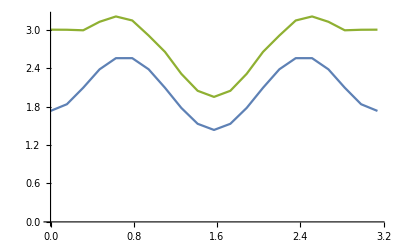

```mathematica
ListLinePlot[{altrdmean,rudinshapiro,altrdmax}]
```

## dt = pi/8 kick*after

### data

```mathematica
kacdatars8={-0.000000000000000000*10^+00,2.000000000000000000*10^+00,2.398404964790533889*10^+00,2.398404964790534777*10^+00,2.398404964790534777*10^+00,2.769031713829400054*10^+00,2.769031713829399166*10^+00,2.769031713829399610*10^+00,2.714859631909449789*10^+00,1.435539529221185440*10^+00,2.233308640386463040*10^+00,2.233308640386463040*10^+00,3.343521875817385247*10^+00,3.343521875817383915*10^+00,3.343521875817384803*10^+00,3.343521875817384359*10^+00,3.343521875817383471*10^+00,3.314719568395871008*10^+00,2.714859631909447124*10^+00,2.714859631909448012*10^+00,2.714859631909447124*10^+00,2.837527072564845376*10^+00,2.837527072564846264*10^+00,2.837527072564844488*10^+00,2.837527072564844488*10^+00,2.837527072564847597*10^+00,2.283449125832060389*10^+00,2.283449125832061277*10^+00,1.980165544722974680*10^+00,3.314719568395867011*10^+00,3.314719568395866567*10^+00,3.314719568395866567*10^+00,3.317964675627838034*10^+00,2.337504713740056417*10^+00,2.164500358436884486*10^+00,2.164500358436884930*10^+00,2.164500358436884486*10^+00,6.208608778065443090*10^-01,6.208608778065440870*10^-01,6.208608778065444200*10^-01,2.215683728838912625*10^+00,2.797664392602566608*10^+00,3.284561163368291403*10^+00,3.284561163368291403*10^+00,2.950027145850905530*10^+00,2.695044487356334173*10^+00,2.695044487356333285*10^+00,2.695044487356334173*10^+00,2.800618706189545115*10^+00,1.686063380365277364*10^+00,2.177516134151476823*10^+00,2.177516134151477711*10^+00,2.177516134151476823*10^+00,3.131668762128348327*10^+00,3.131668762128348327*10^+00,3.131668762128347883*10^+00,3.131668762128347439*10^+00,2.218823808877056436*10^+00,7.932553838259119861*10^-01,7.932553838259127632*10^-01,2.309429669070391711*10^+00,1.686063380365279363*10^+00,1.686063380365278919*10^+00,1.686063380365278919*10^+00,1.686063380365278697*10^+00,2.177516134151479044*10^+00,3.131668762128347439*10^+00,3.131668762128346106*10^+00,3.131668762128346106*10^+00,2.818789045506057356*10^+00,2.818789045506057356*10^+00,2.818789045506056912*10^+00,2.501031584320952739*10^+00,3.124502375365517004*10^+00,3.370563780715183810*10^+00,3.370563780715183810*10^+00,3.749773839319442192*10^+00,2.678239186819945772*10^+00,2.678239186819944884*10^+00,2.678239186819946660*10^+00,2.678239186819945328*10^+00,1.735534032693289319*10^+00,2.501031584320948298*10^+00,2.501031584320948298*10^+00,2.501031584320948298*10^+00,2.050545941499533065*10^+00,2.050545941499533509*10^+00,2.050545941499533509*10^+00,2.050545941499533509*10^+00,2.374510901025980836*10^+00,2.492932210433848716*10^+00,2.492932210433848272*10^+00,2.385192945643734408*10^+00,1.735534032693286211*10^+00,1.735534032693287099*10^+00,1.735534032693287543*10^+00,1.735534032693287099*10^+00,2.501031584320949186*10^+00,2.050545941499532621*10^+00,2.050545941499533065*10^+00,2.050545941499532621*10^+00,2.769024409532374609*10^+00,2.769024409532373276*10^+00,2.769024409532373276*10^+00,2.804972187390625038*10^+00,2.318408459854838455*10^+00,2.513239641162793525*10^+00,2.513239641162793525*10^+00,2.454203710661292170*10^+00,2.865277367740646675*10^+00,2.865277367740646675*10^+00,2.865277367740645342*10^+00,2.107117934965812900*10^+00,1.868590031165069831*10^+00,3.112021391521908154*10^+00,3.112021391521907265*10^+00,3.112021391521908154*10^+00,2.797298181980763854*10^+00,2.797298181980764298*10^+00,2.797298181980762521*10^+00,2.797298181980764742*10^+00,3.295090489605554840*10^+00,2.681033416745262521*10^+00,2.681033416745260300*10^+00,1.483897387911876864*10^+00,1.868590031165065612*10^+00,1.868590031165065390*10^+00,1.868590031165066279*10^+00,2.475752128104713456*10^+00,1.067405572250573087*10^+00,2.317746775099012169*10^+00,2.317746775099011280*10^+00,2.317746775099013945*10^+00,2.143943846981234191*10^+00,2.143943846981234191*10^+00,2.143943846981234636*10^+00,2.911869076949558099*10^+00,1.941950387125750410*10^+00,9.196696967843988046*10^-01,9.196696967843989157*10^-01,2.272180841861465073*10^+00,1.983753415845030288*10^+00,1.983753415845030510*10^+00,1.983753415845030510*10^+00,1.983753415845030066*10^+00,2.694912592341541568*10^+00,2.911869076949559432*10^+00,2.911869076949558544*10^+00,2.911869076949557655*10^+00,3.637686647308656429*10^+00,3.637686647308657761*10^+00,3.637686647308656429*10^+00,3.637686647308656429*10^+00,2.801921336975465415*10^+00,2.739651451004454508*10^+00,2.739651451004455840*10^+00,2.025056373289642941*10^+00,2.694912592341546009*10^+00,2.694912592341546453*10^+00,2.694912592341545565*10^+00,3.104096421632442482*10^+00,2.841971869393058014*10^+00,2.454209670760151951*10^+00,2.454209670760152839*10^+00,2.454209670760151951*10^+00,3.646718990591057974*10^+00,3.646718990591057974*10^+00,3.646718990591057974*10^+00,3.516078923167647918*10^+00,2.146535832338924976*10^+00,2.461732224921133305*10^+00,2.461732224921131973*10^+00,2.541747546110302292*10^+00,2.589012023267879936*10^+00,2.589012023267881712*10^+00,2.589012023267881712*10^+00,3.310196678495799461*10^+00,2.711157150386434900*10^+00,2.993531751054907541*10^+00,2.993531751054907541*10^+00,2.993531751054907541*10^+00,2.631563898425311354*10^+00,2.631563898425311354*10^+00,2.631563898425311798*10^+00,2.631563898425310466*10^+00,1.981447185954818391*10^+00,3.448946781091009495*10^+00,3.448946781091009495*10^+00,2.282405143616839105*10^+00,2.711157150386429127*10^+00,2.711157150386428683*10^+00,2.711157150386429127*10^+00,2.094771079179849504*10^+00,2.387841080885168665*10^+00,2.679119435286840822*10^+00,2.679119435286840378*10^+00,2.679119435286840822*10^+00,2.730837663684467120*10^+00,2.730837663684466232*10^+00,2.730837663684467120*10^+00,2.722912528242654327*10^-14,1.929680324037557071*10^+00,2.313263142520595395*10^+00,2.313263142517538284*10^+00,2.313263142520595395*10^+00,2.730518948053192396*10^+00,2.730518948053163975*10^+00,2.730518948053191952*10^+00,2.789036626813686137*10^+00,1.701407631308324619*10^+00,2.412834599386132428*10^+00,2.412834599385492496*10^+00,3.328790327492006984*10^+00,3.363601607709147956*10^+00,3.363601607709146624*10^+00,3.363601607709147956*10^+00,3.363601607709147068*10^+00,3.312883070867417068*10^+00,2.724939401962401142*10^+00,2.724939401961822050*10^+00,2.724939401962402030*10^+00,2.816337593475469525*10^+00,2.816337593475514378*10^+00,2.816337593475469081*10^+00,2.816337593475514378*10^+00,2.777162030341852716*10^+00,2.334459638927144365*10^+00,2.334459638927145697*10^+00,2.083156784557620878*10^+00,3.303349172780289500*10^+00,3.303349172780289500*10^+00,3.303349172780289056*10^+00,3.297307632530114940*10^+00,2.493374885908797189*10^+00,2.316496360043259095*10^+00,2.316496360043258207*10^+00,2.316496360043259095*10^+00,8.664819528233255186*10^-01,8.664819528232495793*10^-01,8.664819528233260737*10^-01,2.380817987111242928*10^+00,2.866900019084111850*10^+00,3.248359360523714212*10^+00,3.248359360523714656*10^+00,2.962289496225388064*10^+00,2.648418445442122238*10^+00,2.648418445442122238*10^+00,2.648418445442122682*10^+00,2.803442977503418199*10^+00,1.786448895910416335*10^+00,2.288289398801599095*10^+00,2.288289398801598651*10^+00,2.288289398801598651*10^+00,3.140481937445267047*10^+00,3.140481937445267047*10^+00,3.140481937445266158*10^+00,3.140481937445267935*10^+00,2.372009072935123086*10^+00,1.053363457568750272*10^+00,1.053363457568751382*10^+00,2.475771799118688499*10^+00,1.842302469277957933*10^+00,1.842302469277958821*10^+00,1.842302469277959043*10^+00,1.842302469277958599*10^+00,2.264042409327453598*10^+00,3.069167693358725302*10^+00,3.069167693358726190*10^+00,3.069167693358725302*10^+00,2.745841404168678057*10^+00,2.745841404168679833*10^+00,2.745841404168676725*10^+00,2.497945301118273953*10^+00,3.081010440529323269*10^+00,3.334072699680130647*10^+00,3.334072699680131535*10^+00,3.726028604992912108*10^+00,2.714938454411032875*10^+00,2.714938454411578661*10^+00,2.714938454411032431*10^+00,2.714938454411577329*10^+00,1.863643476482044647*10^+00,2.616023095474141247*10^+00,2.616023095474141691*10^+00,2.616023095474140359*10^+00,2.083514945163375209*10^+00,2.083514945163375209*10^+00,2.083514945163375653*10^+00,2.083514945163375209*10^+00,2.300999662052474637*10^+00,2.386077194592396644*10^+00,2.386077194592396644*10^+00,2.277765267365515545*10^+00,1.592229818394763630*10^+00,1.592229818394764962*10^+00,1.592229818394764962*10^+00,1.592229818394764518*10^+00,2.483473974803222628*10^+00,2.196293548216530223*10^+00,2.196293548216530667*10^+00,2.196293548216528890*10^+00,2.792146904543920449*10^+00,2.792146904543920893*10^+00,2.792146904543920893*10^+00,2.845560005073505039*10^+00,2.465701982867405384*10^+00,2.636662074116145948*10^+00,2.636662074116146393*10^+00,2.559417792932773938*10^+00,2.892477613652786328*10^+00,2.892477613652787216*10^+00,2.892477613652786328*10^+00,2.228039915617502587*10^+00,1.974319576296251766*10^+00,3.093532851224008784*10^+00,3.093532851224008784*10^+00,3.093532851224007896*10^+00,2.767474461028540222*10^+00,2.767474461028575305*10^+00,2.767474461028539778*10^+00,2.767474461028576194*10^+00,3.261056834442479513*10^+00,2.664575224874049297*10^+00,2.664575224874047521*10^+00,1.625461478265411097*10^+00,1.922385278589671120*10^+00,1.922385278589672231*10^+00,1.922385278589671787*10^+00,2.551434902053161480*10^+00,1.259893835024754383*10^+00,2.413854574156984789*10^+00,2.413854574156985233*10^+00,2.413854574156984345*10^+00,2.271415217532364750*10^+00,2.271415217532364750*10^+00,2.271415217532364750*10^+00,2.915756912677991419*10^+00,2.033630216681969749*10^+00,1.060671267669258455*10^+00,1.060671267669258677*10^+00,2.266074849049044104*10^+00,2.044767906258317058*10^+00,2.044767906258317058*10^+00,2.044767906258316614*10^+00,2.044767906258316614*10^+00,2.793943743949536263*10^+00,2.914143867853835168*10^+00,2.914143867853836056*10^+00,2.914143867853835168*10^+00,3.578149233259757089*10^+00,3.578149233259757089*10^+00,3.578149233259756645*10^+00,3.578149233259756645*10^+00,2.859044406139009897*10^+00,2.885255357315736013*10^+00,2.885255357315735569*10^+00,2.242606234540809762*10^+00,2.854627057170184834*10^+00,2.854627057170185722*10^+00,2.854627057170185278*10^+00,3.079375408754705390*10^+00,2.881272855335446081*10^+00,2.549114815215146379*10^+00,2.549114815215146379*10^+00,2.549114815215145047*10^+00,3.603781355287167365*10^+00,3.603781355287167809*10^+00,3.603781355287167365*10^+00,3.505313348097474080*10^+00,2.280133926677749834*10^+00,2.582938584215282773*10^+00,2.582938584215282773*10^+00,2.580641159592767409*10^+00,2.688911485613123098*10^+00,2.688911485613123098*10^+00,2.688911485613121766*10^+00,3.363493503555698982*10^+00,2.751655503514542467*10^+00,2.961502605669057431*10^+00,2.961502605669057431*10^+00,2.961502605669057875*10^+00,2.688043449720554090*10^+00,2.688043449720552758*10^+00,2.688043449720552758*10^+00,2.688043449720552758*10^+00,2.166530104672358625*10^+00,3.440108514893665426*10^+00,3.440108514893664982*10^+00,2.338539818701043771*10^+00,2.708965427730496867*10^+00,2.708965427730495978*10^+00,2.708965427730495978*10^+00,2.140629647481559594*10^+00,2.404753244502488840*10^+00,2.743057165471999959*10^+00,2.743057165471999959*10^+00,2.743057165471999959*10^+00,2.811137140807777879*10^+00,2.811137140807776991*10^+00,2.811137140807777435*10^+00,-9.610279511444755881*10^-16,1.729030204872845200*10^+00,2.086752672442499179*10^+00,2.086752672442499179*10^+00,2.086752672442498735*10^+00,2.623295501941308228*10^+00,2.623295501941306895*10^+00,2.623295501941307784*10^+00,2.951731397072172136*10^+00,2.189887390241048948*10^+00,2.650390234175482806*10^+00,2.650390234175485027*10^+00,3.316835132533671349*10^+00,3.374564869404411915*10^+00,3.374564869404411915*10^+00,3.374564869404411471*10^+00,3.374564869404411027*10^+00,3.288819868031961136*10^+00,2.753999083060428177*10^+00,2.753999083060429065*10^+00,2.753999083060428177*10^+00,2.785959496651329914*10^+00,2.785959496651329026*10^+00,2.785959496651329914*10^+00,2.785959496651330802*10^+00,2.705712263892355196*10^+00,2.474209539311997830*10^+00,2.474209539311997830*10^+00,2.390954933134277649*10^+00,3.266809406658537807*10^+00,3.266809406658538695*10^+00,3.266809406658537807*10^+00,3.273313592607756117*10^+00,2.638960388984039174*10^+00,2.607066530282403871*10^+00,2.607066530282402539*10^+00,2.607066530282402983*10^+00,1.291117552056448403*10^+00,1.291117552056448625*10^+00,1.291117552056448403*10^+00,2.743519647448902532*10^+00,2.989284178454492569*10^+00,3.177104167620698583*10^+00,3.177104167620698139*10^+00,2.969079299392053173*10^+00,2.523980793121033628*10^+00,2.523980793121033628*10^+00,2.523980793121034072*10^+00,2.813347229597974231*10^+00,2.034283501428562513*10^+00,2.539700090119163534*10^+00,2.539700090119163534*10^+00,2.539700090119163089*10^+00,3.119000679803285436*10^+00,3.119000679803284548*10^+00,3.119000679803284548*10^+00,3.119000679803283660*10^+00,2.539902350187807745*10^+00,1.475200855225237362*10^+00,1.475200855225236474*10^+00,2.756579026855611403*10^+00,2.119589455498565922*10^+00,2.119589455498565922*10^+00,2.119589455498566810*10^+00,2.119589455498566366*10^+00,2.387831057539234081*10^+00,2.927236806456029683*10^+00,2.927236806456028795*10^+00,2.927236806456027907*10^+00,2.575782393801354875*10^+00,2.575782393801354431*10^+00,2.575782393801354875*10^+00,2.535560793362671816*10^+00,2.981979124428966177*10^+00,3.230350330719373719*10^+00,3.230350330719373719*10^+00,3.612354767035968361*10^+00,2.765342079333556136*10^+00,2.765342079333556580*10^+00,2.765342079333556136*10^+00,2.765342079333556136*10^+00,2.088858247166791138*10^+00,2.848936014295967212*10^+00,2.848936014295967212*10^+00,2.848936014295967212*10^+00,2.171660038557542638*10^+00,2.171660038557542638*10^+00,2.171660038557542638*10^+00,2.171660038557542638*10^+00,2.116951727989516474*10^+00,2.119753197785115173*10^+00,2.119753197785116505*10^+00,2.026145812266269441*10^+00,1.276045629648055568*10^+00,1.276045629648057789*10^+00,1.276045629648056234*10^+00,1.276045629648054458*10^+00,2.437246952566368918*10^+00,2.486116210087064182*10^+00,2.486116210087064626*10^+00,2.486116210087064626*10^+00,2.851042536129099858*10^+00,2.851042536129098970*10^+00,2.851042536129099414*10^+00,2.943315870626943997*10^+00,2.745701177563875106*10^+00,2.823130059084918209*10^+00,2.823130059084918209*10^+00,2.730577138484542754*10^+00,2.924283550563743006*10^+00,2.924283550563742118*10^+00,2.924283550563742118*10^+00,2.520121829814315095*10^+00,2.259893057249508175*10^+00,3.042181252382680334*10^+00,3.042181252382681222*10^+00,3.042181252382678558*10^+00,2.689992101980345218*10^+00,2.689992101980346106*10^+00,2.689992101980344330*10^+00,2.689992101980346106*10^+00,3.168606611149956898*10^+00,2.648564228365502426*10^+00,2.648564228365501982*10^+00,1.925223050575132877*10^+00,2.098359166829779632*10^+00,2.098359166829778744*10^+00,2.098359166829779188*10^+00,2.680121290452837091*10^+00,1.575185107100525173*10^+00,2.540955617788112075*10^+00,2.540955617788112075*10^+00,2.540955617788111187*10^+00,2.501636628021239872*10^+00,2.501636628021239872*10^+00,2.501636628021239428*10^+00,2.899970653734465831*10^+00,2.216466434961951837*10^+00,1.375537144351011154*10^+00,1.375537144351010266*10^+00,2.200463308502327298*10^+00,2.153274787579808169*10^+00,2.153274787579807725*10^+00,2.153274787579809058*10^+00,2.153274787579808169*10^+00,2.979468149677795274*10^+00,2.923055284926469710*10^+00,2.923055284926469266*10^+00,2.923055284926468822*10^+00,3.421115738009604001*10^+00,3.421115738009604446*10^+00,3.421115738009603557*10^+00,3.421115738009602669*10^+00,2.983303420575126985*10^+00,2.987156475899654495*10^+00,2.987156475899654495*10^+00,2.617044040804543670*10^+00,3.077456838235512748*10^+00,3.077456838235512748*10^+00,3.077456838235511860*10^+00,3.049516253510333286*10^+00,2.895876326354799080*10^+00,2.694881048262430134*10^+00,2.694881048262429246*10^+00,2.694881048262429690*10^+00,3.453545479551383579*10^+00,3.453545479551384911*10^+00,3.453545479551382247*10^+00,3.454480331571132545*10^+00,2.569746623797755092*10^+00,2.852694944203371552*10^+00,2.852694944203371552*10^+00,2.658219515087662632*10^+00,2.899280135349511678*10^+00,2.899280135349512122*10^+00,2.899280135349510790*10^+00,3.423965007206471345*10^+00,2.837694569691027180*10^+00,2.894034591547712587*10^+00,2.894034591547712587*10^+00,2.894034591547711699*10^+00,2.859110978444375561*10^+00,2.859110978444375561*10^+00,2.859110978444376006*10^+00,2.859110978444376006*10^+00,2.494383733446275286*10^+00,3.396974735345301255*10^+00,3.396974735345301255*10^+00,2.462317071095630805*10^+00,2.685706663274003869*10^+00,2.685706663274003869*10^+00,2.685706663274003425*10^+00,2.253343334297483125*10^+00,2.457473713991855213*10^+00,2.858121718781740928*10^+00,2.858121718781740483*10^+00,2.858121718781741372*10^+00,2.902743893179542400*10^+00,2.902743893179542845*10^+00,2.902743893179541956*10^+00,9.610279511444749964*10^-16,1.427593131110274305*10^+00,1.785373400151494261*10^+00,1.785373400151494261*10^+00,1.785373400151495149*10^+00,2.496478558615757848*10^+00,2.496478558615758736*10^+00,2.496478558615757848*10^+00,3.012427033137295318*10^+00,2.566584589342639777*10^+00,2.732484280283317357*10^+00,2.732484280283317357*10^+00,3.260140344056952966*10^+00,3.349472913904518734*10^+00,3.349472913904518290*10^+00,3.349472913904517846*10^+00,3.349472913904517846*10^+00,3.229329687314521635*10^+00,2.867721564374908549*10^+00,2.867721564374907661*10^+00,2.867721564374908549*10^+00,2.802376384814205590*10^+00,2.802376384814206034*10^+00,2.802376384814205146*10^+00,2.802376384814205146*10^+00,2.603716145294185935*10^+00,2.595681614654413938*10^+00,2.595681614654414382*10^+00,2.749286347726134672*10^+00,3.180220517857768048*10^+00,3.180220517857768492*10^+00,3.180220517857766716*10^+00,3.273435748478501495*10^+00,2.628940235958512339*10^+00,2.843646125769197841*10^+00,2.843646125769196509*10^+00,2.843646125769196953*10^+00,1.733288906765805493*10^+00,1.733288906765805937*10^+00,1.733288906765805715*10^+00,3.049421135427400564*10^+00,3.015046823109080787*10^+00,3.101977223291966013*10^+00,3.101977223291966013*10^+00,2.935748075146483949*10^+00,2.351686136114794934*10^+00,2.351686136114794934*10^+00,2.351686136114795822*10^+00,2.823690733881602632*10^+00,2.265028493626357164*10^+00,2.732807465127199631*10^+00,2.732807465127199631*10^+00,2.732807465127200075*10^+00,3.055878412399786637*10^+00,3.055878412399786193*10^+00,3.055878412399786193*10^+00,3.055878412399786193*10^+00,2.573924516040687838*10^+00,1.878408237815751836*10^+00,1.878408237815752502*10^+00,2.988826316576530751*10^+00,2.416298699934564809*10^+00,2.416298699934564365*10^+00,2.416298699934564809*10^+00,2.416298699934563476*10^+00,2.444314947983940112*10^+00,2.795231136113551784*10^+00,2.795231136113551784*10^+00,2.795231136113550896*10^+00,2.403691242661240679*10^+00,2.403691242661240679*10^+00,2.403691242661239791*10^+00,2.613060451088482505*10^+00,2.894564096667714637*10^+00,3.074686949930216961*10^+00,3.074686949930217850*10^+00,3.366983034370760297*10^+00,2.744578182235965169*10^+00,2.744578182235963837*10^+00,2.744578182235963393*10^+00,2.744578182235963393*10^+00,2.343681890807537194*10^+00,3.014797499478780729*10^+00,3.014797499478779841*10^+00,3.014797499478779841*10^+00,2.294434241031237498*10^+00,2.294434241031237498*10^+00,2.294434241031237054*10^+00,2.294434241031237054*10^+00,1.918573925828697568*10^+00,1.816067388907304458*10^+00,1.816067388907304014*10^+00,1.886205969770668123*10^+00,1.055969711133744049*10^+00,1.055969711133743605*10^+00,1.055969711133743605*10^+00,1.055969711133744049*10^+00,2.356494634550831080*10^+00,2.787524043270825480*10^+00,2.787524043270825480*10^+00,2.787524043270825480*10^+00,2.924790873797403101*10^+00,2.924790873797402657*10^+00,2.924790873797402213*10^+00,3.010279183560529592*10^+00,3.002417243785565848*10^+00,2.875544192548715738*10^+00,2.875544192548714406*10^+00,2.855933387947391822*10^+00,2.895834147989772678*10^+00,2.895834147989773122*10^+00,2.895834147989772234*10^+00,2.828060825060965122*10^+00,2.496260429324284047*10^+00,2.971785707275688804*10^+00,2.971785707275687916*10^+00,2.971785707275688360*10^+00,2.594582509086544420*10^+00,2.594582509086545308*10^+00,2.594582509086544864*10^+00,2.594582509086544420*10^+00,3.044157138714001398*10^+00,2.623869809290032329*10^+00,2.623869809290032329*10^+00,2.178279631151424311*10^+00,2.309726424081277596*10^+00,2.309726424081278040*10^+00,2.309726424081277152*10^+00,2.864333261286537979*10^+00,1.855368230996464085*10^+00,2.584005656722368371*10^+00,2.584005656722368371*10^+00,2.584005656722367927*10^+00,2.691159518471309742*10^+00,2.691159518471310186*10^+00,2.691159518471310186*10^+00,2.962115055642033923*10^+00,2.476641913660004413*10^+00,1.674776648180243965*10^+00,1.674776648180244187*10^+00,2.031552396763861346*10^+00,2.195026928351619055*10^+00,2.195026928351619055*10^+00,2.195026928351618611*10^+00,2.195026928351618167*10^+00,3.120230786589623051*10^+00,2.907663264472407860*10^+00,2.907663264472408748*10^+00,2.907663264472408304*10^+00,3.197482678305588077*10^+00,3.197482678305588522*10^+00,3.197482678305587189*10^+00,3.197482678305588522*10^+00,3.023657035669667703*10^+00,2.948158424235405750*10^+00,2.948158424235405306*10^+00,2.904463547832289994*10^+00,3.182143356709613347*10^+00,3.182143356709614235*10^+00,3.182143356709613791*10^+00,2.947638295620087945*10^+00,2.789830229486402580*10^+00,2.763874886265127895*10^+00,2.763874886265127451*10^+00,2.763874886265127007*10^+00,3.187605672759321607*10^+00,3.187605672759322051*10^+00,3.187605672759320719*10^+00,3.336369972501323389*10^+00,2.819890032077814190*10^+00,3.131617224954276857*10^+00,3.131617224954276857*10^+00,2.730798916460231318*10^+00,3.042774770123743089*10^+00,3.042774770123741312*10^+00,3.042774770123741312*10^+00,3.372937201880107594*10^+00,2.922171210955153420*10^+00,2.843414578432251094*10^+00,2.843414578432250650*10^+00,2.843414578432249762*10^+00,3.060253531990654974*10^+00,3.060253531990655418*10^+00,3.060253531990654530*10^+00,3.060253531990654086*10^+00,2.754341929411503909*10^+00,3.309036324974085286*10^+00,3.309036324974084398*10^+00,2.601872631343908004*10^+00,2.589663043100465689*10^+00,2.589663043100464357*10^+00,2.589663043100465245*10^+00,2.391092510018152595*10^+00,2.541927475926140545*10^+00,2.943399783944895098*10^+00,2.943399783944893322*10^+00,2.943399783944894210*10^+00,2.861454586408724410*10^+00,2.861454586408724410*10^+00,2.861454586408723522*10^+00,4.805139755722374982*10^-16,1.070009614893122851*10^+00,1.499957157121726725*10^+00,1.499957157121726947*10^+00,1.499957157121726059*10^+00,2.360855972646970002*10^+00,2.360855972646969114*10^+00,2.360855972646967782*10^+00,2.931801281313387797*10^+00,2.718714751413592090*10^+00,2.667827073000232474*10^+00,2.667827073000231586*10^+00,3.179666951361654004*10^+00,3.319553870721641875*10^+00,3.319553870721640543*10^+00,3.319553870721640543*10^+00,3.319553870721640543*10^+00,3.184407542342274411*10^+00,3.084973794112130463*10^+00,3.084973794112130019*10^+00,3.084973794112129575*10^+00,2.869675301071862528*10^+00,2.869675301071862084*10^+00,2.869675301071862528*10^+00,2.869675301071862972*10^+00,2.486904856828330068*10^+00,2.661279774722003832*10^+00,2.661279774722002944*10^+00,2.989967057929432848*10^+00,3.064510689224238416*10^+00,3.064510689224237971*10^+00,3.064510689224237527*10^+00,3.244131189150468941*10^+00,2.514862722319274546*10^+00,2.943630598360841510*10^+00,2.943630598360841955*10^+00,2.943630598360841066*10^+00,2.147869656940454952*10^+00,2.147869656940455840*10^+00,2.147869656940455396*10^+00,3.235683866795243446*10^+00,2.929722431246291059*10^+00,3.025876784135766773*10^+00,3.025876784135766773*10^+00,2.883359407493017113*10^+00,2.209572720525857292*10^+00,2.209572720525857736*10^+00,2.209572720525857292*10^+00,2.821012087401866708*10^+00,2.408821973386890303*10^+00,2.791279505231187841*10^+00,2.791279505231187397*10^+00,2.791279505231186508*10^+00,2.930492026010673268*10^+00,2.930492026010673268*10^+00,2.930492026010673268*10^+00,2.930492026010672824*10^+00,2.543368843827535031*10^+00,2.218400219576696752*10^+00,2.218400219576696308*10^+00,3.143175794219912778*10^+00,2.663835911568235737*10^+00,2.663835911568235293*10^+00,2.663835911568235293*10^+00,2.663835911568234849*10^+00,2.494452519581849881*10^+00,2.724077455397929448*10^+00,2.724077455397928560*10^+00,2.724077455397928560*10^+00,2.327800242852777313*10^+00,2.327800242852776869*10^+00,2.327800242852776869*10^+00,2.738527817388811236*10^+00,2.881648458659339607*10^+00,2.947379296129108539*10^+00,2.947379296129108095*10^+00,3.029212903397773271*10^+00,2.658160531110697722*10^+00,2.658160531110695946*10^+00,2.658160531110695946*10^+00,2.658160531110695946*10^+00,2.594626574736230040*10^+00,3.055590689466539001*10^+00,3.055590689466539445*10^+00,3.055590689466539001*10^+00,2.392234360279635652*10^+00,2.392234360279637428*10^+00,2.392234360279634320*10^+00,2.392234360279635652*10^+00,1.856568368497989674*10^+00,1.656070275834466532*10^+00,1.656070275834466532*10^+00,1.866480249326521790*10^+00,1.161086259964193124*10^+00,1.161086259964193346*10^+00,1.161086259964192235*10^+00,1.161086259964192902*10^+00,2.294634594827316576*10^+00,2.978414908456640919*10^+00,2.978414908456641363*10^+00,2.978414908456640475*10^+00,2.979765538920005952*10^+00,2.979765538920005064*10^+00,2.979765538920005508*10^+00,3.012276314392865029*10^+00,3.133993382623414536*10^+00,2.827441781047589586*10^+00,2.827441781047590474*10^+00,2.941432490345623485*10^+00,2.794853010275492711*10^+00,2.794853010275492267*10^+00,2.794853010275492267*10^+00,3.002199110166269946*10^+00,2.627830875887165796*10^+00,2.905394081809862694*10^+00,2.905394081809863138*10^+00,2.905394081809862694*10^+00,2.510409100143665917*10^+00,2.510409100143665029*10^+00,2.510409100143664141*10^+00,2.510409100143664141*10^+00,2.909858298971204960*10^+00,2.589644782996778360*10^+00,2.589644782996779249*10^+00,2.324521689361487731*10^+00,2.447877496310066903*10^+00,2.447877496310067347*10^+00,2.447877496310067791*10^+00,2.995871501508243551*10^+00,2.153653399427442050*10^+00,2.560904255584528944*10^+00,2.560904255584528944*10^+00,2.560904255584529388*10^+00,2.807558044345248138*10^+00,2.807558044345249026*10^+00,2.807558044345248138*10^+00,3.070859636934439418*10^+00,2.732552037247822252*10^+00,1.890009067937074239*10^+00,1.890009067937074239*10^+00,1.836663555124141922*10^+00,2.145211504159201699*10^+00,2.145211504159201255*10^+00,2.145211504159202143*10^+00,2.145211504159201255*10^+00,3.154299992816820719*10^+00,2.904114063272385415*10^+00,2.904114063272385415*10^+00,2.904114063272385415*10^+00,2.992481390220270043*10^+00,2.992481390220269155*10^+00,2.992481390220270043*10^+00,2.992481390220270043*10^+00,3.003389700981076160*10^+00,2.846807496437211427*10^+00,2.846807496437209650*10^+00,3.063296488879613477*10^+00,3.165898629220614158*10^+00,3.165898629220613714*10^+00,3.165898629220613714*10^+00,2.785826072376741180*10^+00,2.597463592464484883*10^+00,2.698922574920865181*10^+00,2.698922574920863404*10^+00,2.698922574920864292*10^+00,2.869487911172042605*10^+00,2.869487911172042605*10^+00,2.869487911172042605*10^+00,3.158545028129674748*10^+00,2.977189504775115569*10^+00,3.290549301376045399*10^+00,3.290549301376045843*10^+00,2.760772292935965488*10^+00,3.069104713798981976*10^+00,3.069104713798981976*10^+00,3.069104713798979756*10^+00,3.214256109599568756*10^+00,2.941469465891485058*10^+00,2.801116435302631213*10^+00,2.801116435302632546*10^+00,2.801116435302631658*10^+00,3.195574608631843283*10^+00,3.195574608631843727*10^+00,3.195574608631843283*10^+00,3.195574608631842395*10^+00,2.868473522825349953*10^+00,3.198439809972648984*10^+00,3.198439809972648096*10^+00,2.710895921658379226*10^+00,2.429891406966552481*10^+00,2.429891406966552481*10^+00,2.429891406966552481*10^+00,2.524853072324771741*10^+00,2.655895118881855144*10^+00,2.924456802743058859*10^+00,2.924456802743058415*10^+00,2.924456802743058859*10^+00,2.716090235601297032*10^+00,2.716090235601296143*10^+00,2.716090235601296143*10^+00,3.203426503814917641*10^-16,7.091578053305397367*10^-01,1.263977579813405416*10^+00,1.263977579813405860*10^+00,1.263977579813404750*10^+00,2.197668167360891545*10^+00,2.197668167360891545*10^+00,2.197668167360890656*10^+00,2.712922859740127812*10^+00,2.691891665685866908*10^+00,2.493219857097728642*10^+00,2.493219857097729086*10^+00,3.070929095323000624*10^+00,3.298394326132815024*10^+00,3.298394326132814580*10^+00,3.298394326132815024*10^+00,3.298394326132814136*10^+00,3.180975420924733843*10^+00,3.266430936010591424*10^+00,3.266430936010590536*10^+00,3.266430936010590536*10^+00,2.940256280851625270*10^+00,2.940256280851625714*10^+00,2.940256280851623938*10^+00,2.940256280851624382*10^+00,2.380968865511591037*10^+00,2.639558531158638477*10^+00,2.639558531158638033*10^+00,3.030928253842258613*10^+00,2.902837569301764287*10^+00,2.902837569301764287*10^+00,2.902837569301762954*10^+00,3.118094467413513371*10^+00,2.457974162442119415*10^+00,2.920863539347628546*10^+00,2.920863539347629434*10^+00,2.920863539347628990*10^+00,2.402493214408397915*10^+00,2.402493214408399247*10^+00,2.402493214408398803*10^+00,3.251995587685795996*10^+00,2.832335137455371576*10^+00,2.972633584632074832*10^+00,2.972633584632075276*10^+00,2.841309621411812092*10^+00,2.113856324428592171*10^+00,2.113856324428591726*10^+00,2.113856324428591282*10^+00,2.799266590412330835*10^+00,2.445949750917563836*10^+00,2.702124292777011494*10^+00,2.702124292777010606*10^+00,2.702124292777011050*10^+00,2.830609840248937470*10^+00,2.830609840248936138*10^+00,2.830609840248937470*10^+00,2.830609840248937026*10^+00,2.588453882197423894*10^+00,2.480153682217866695*10^+00,2.480153682217866695*10^+00,3.196520537923800642*10^+00,2.851335575752957041*10^+00,2.851335575752957041*10^+00,2.851335575752956153*10^+00,2.851335575752956153*10^+00,2.559542617543380416*10^+00,2.705644352206463044*10^+00,2.705644352206463044*10^+00,2.705644352206463044*10^+00,2.367390258856077345*10^+00,2.367390258856076457*10^+00,2.367390258856076457*10^+00,2.859405401863873486*10^+00,2.913451072778657114*10^+00,2.859360734818487959*10^+00,2.859360734818487959*10^+00,2.706744325581592836*10^+00,2.550747162818503888*10^+00,2.550747162818502556*10^+00,2.550747162818503444*10^+00,2.550747162818502556*10^+00,2.767103577246165180*10^+00,2.956696183364936115*10^+00,2.956696183364936559*10^+00,2.956696183364935671*10^+00,2.417420758655663970*10^+00,2.417420758655664415*10^+00,2.417420758655664415*10^+00,2.417420758655663970*10^+00,1.968853407381738752*10^+00,1.692736669159322860*10^+00,1.692736669159323970*10^+00,1.999946742822085177*10^+00,1.429472523143996865*10^+00,1.429472523143997087*10^+00,1.429472523143996865*10^+00,1.429472523143996421*10^+00,2.253321828566963170*10^+00,3.023753925814654409*10^+00,3.023753925814653964*10^+00,3.023753925814654409*10^+00,2.953748172636633029*10^+00,2.953748172636633029*10^+00,2.953748172636633029*10^+00,2.913844970384855237*10^+00,3.120600334764867423*10^+00,2.763777907354752372*10^+00,2.763777907354752372*10^+00,2.960128802664915959*10^+00,2.705681035705247872*10^+00,2.705681035705248760*10^+00,2.705681035705247872*10^+00,3.045746351299857047*10^+00,2.660165437868030391*10^+00,2.867214082649661933*10^+00,2.867214082649661933*10^+00,2.867214082649662377*10^+00,2.481382630764775943*10^+00,2.481382630764776831*10^+00,2.481382630764776387*10^+00,2.481382630764776831*10^+00,2.803770688040737813*10^+00,2.534922703727664928*10^+00,2.534922703727664484*10^+00,2.353722837802520118*10^+00,2.492818072050737577*10^+00,2.492818072050738465*10^+00,2.492818072050738465*10^+00,3.047349463932801150*10^+00,2.423774772018451262*10^+00,2.505653740148096276*10^+00,2.505653740148095832*10^+00,2.505653740148094943*10^+00,2.835792192422774249*10^+00,2.835792192422774249*10^+00,2.835792192422772473*10^+00,3.082726744272012986*10^+00,2.852982107138411383*10^+00,2.051177676544889916*10^+00,2.051177676544889472*10^+00,1.785954806096590186*10^+00,2.090645389921291120*10^+00,2.090645389921290231*10^+00,2.090645389921291120*10^+00,2.090645389921291120*10^+00,3.087768083633782190*10^+00,2.883000291659706171*10^+00,2.883000291659706171*10^+00,2.883000291659705283*10^+00,2.875908856980984307*10^+00,2.875908856980984307*10^+00,2.875908856980984307*10^+00,2.875908856980984307*10^+00,2.926177197848300882*10^+00,2.837313416980144609*10^+00,2.837313416980143721*10^+00,3.120689626820804197*10^+00,3.106808245138499291*10^+00,3.106808245138499291*10^+00,3.106808245138498847*10^+00,2.666467390354611666*10^+00,2.432988804966725205*10^+00,2.589490447751139790*10^+00,2.589490447751140678*10^+00,2.589490447751139790*10^+00,2.601192095725808784*10^+00,2.601192095725808784*10^+00,2.601192095725807896*10^+00,2.967897665771702886*10^+00,3.014921525138178460*10^+00,3.258253007097895004*10^+00,3.258253007097896337*10^+00,2.739814764535914549*10^+00,3.001094532672086590*10^+00,3.001094532672086590*10^+00,3.001094532672086146*10^+00,3.023064668146485001*10^+00,2.897334627652162986*10^+00,2.723223387340980128*10^+00,2.723223387340978796*10^+00,2.723223387340980128*10^+00,3.196191845395035536*10^+00,3.196191845395035536*10^+00,3.196191845395034647*10^+00,3.196191845395035536*10^+00,2.870198748358317342*10^+00,3.091429020513899673*10^+00,3.091429020513899228*10^+00,2.795365126809670642*10^+00,2.250264149259965318*10^+00,2.250264149259964874*10^+00,2.250264149259964874*10^+00,2.627134279445181519*10^+00,2.771196817529742340*10^+00,2.797032038894369244*10^+00,2.797032038894367911*10^+00,2.797032038894368799*10^+00,2.577811563428014541*10^+00,2.577811563428014541*10^+00,2.577811563428014985*10^+00,-9.610279511444755881*10^-16,3.871470010700649445*10^-01,1.145892345322474304*10^+00,1.145892345322475414*10^+00,1.145892345322475636*10^+00,1.949680243014677350*10^+00,1.949680243014676684*10^+00,1.949680243014676240*10^+00,2.399256549285693652*10^+00,2.523588383257821199*10^+00,2.239933679857669002*10^+00,2.239933679857668558*10^+00,2.951386938371727719*10^+00,3.259295305378294483*10^+00,3.259295305378294483*10^+00,3.259295305378294483*10^+00,3.259295305378293151*10^+00,3.164515712003477699*10^+00,3.336809979223305245*10^+00,3.336809979223306577*10^+00,3.336809979223304801*10^+00,2.973949695616389999*10^+00,2.973949695616389999*10^+00,2.973949695616389999*10^+00,2.973949695616389111*10^+00,2.285925842389525897*10^+00,2.520188305980116894*10^+00,2.520188305980117338*10^+00,2.877577219884015047*10^+00,2.705748442211354909*10^+00,2.705748442211354909*10^+00,2.705748442211354909*10^+00,2.883293680412308824*10^+00,2.518457896897017267*10^+00,2.766869883463459967*10^+00,2.766869883463460411*10^+00,2.766869883463459523*10^+00,2.491183020007883275*10^+00,2.491183020007883275*10^+00,2.491183020007883719*10^+00,3.131149443858660231*10^+00,2.787889391204583234*10^+00,2.930860805114794410*10^+00,2.930860805114795742*10^+00,2.835699501225539265*10^+00,2.104989815575458945*10^+00,2.104989815575458501*10^+00,2.104989815575458501*10^+00,2.747855226892526925*10^+00,2.422128093480228728*10^+00,2.477071769267967127*10^+00,2.477071769267966239*10^+00,2.477071769267967127*10^+00,2.736503911516121601*10^+00,2.736503911516122045*10^+00,2.736503911516122933*10^+00,2.736503911516122045*10^+00,2.703130310020152471*10^+00,2.647879276797688863*10^+00,2.647879276797688419*10^+00,3.160780716455574346*10^+00,2.973925894351276078*10^+00,2.973925894351275190*10^+00,2.973925894351275190*10^+00,2.973925894351274302*10^+00,2.649961404800822429*10^+00,2.730582739398387027*10^+00,2.730582739398386583*10^+00,2.730582739398387915*10^+00,2.469832534477519381*10^+00,2.469832534477519825*10^+00,2.469832534477518493*10^+00,2.945395218465380438*10^+00,2.915984109909020017*10^+00,2.813434659388144077*10^+00,2.813434659388144077*10^+00,2.472141153027894944*10^+00,2.432646525412694327*10^+00,2.432646525412693439*10^+00,2.432646525412693439*10^+00,2.432646525412693883*10^+00,2.811986659605046235*10^+00,2.764246328349686088*10^+00,2.764246328349686088*10^+00,2.764246328349686088*10^+00,2.366865668722294203*10^+00,2.366865668722294203*10^+00,2.366865668722293314*10^+00,2.366865668722293314*10^+00,2.195053348368023904*10^+00,1.883341174664715068*10^+00,1.883341174664715068*10^+00,2.147631026147279965*10^+00,1.709825419679092962*10^+00,1.709825419679093184*10^+00,1.709825419679093184*10^+00,1.709825419679093628*10^+00,2.197762033499067069*10^+00,2.916439395343028984*10^+00,2.916439395343028096*10^+00,2.916439395343028984*10^+00,2.778622781459362479*10^+00,2.778622781459361590*10^+00,2.778622781459361590*10^+00,2.694912407905999174*10^+00,2.969770757668631411*10^+00,2.714136484317651199*10^+00,2.714136484317650755*10^+00,2.907546433511006168*10^+00,2.677291372685972615*10^+00,2.677291372685972171*10^+00,2.677291372685973059*10^+00,2.955987601585433833*10^+00,2.663718322992615128*10^+00,2.864418332783508880*10^+00,2.864418332783508880*10^+00,2.864418332783508880*10^+00,2.517591039049051904*10^+00,2.517591039049051904*10^+00,2.517591039049051904*10^+00,2.517591039049051016*10^+00,2.700812270617688249*10^+00,2.470031350134889614*10^+00,2.470031350134887838*10^+00,2.294248410272869965*10^+00,2.441139444627490551*10^+00,2.441139444627489663*10^+00,2.441139444627490995*10^+00,3.006490776727355652*10^+00,2.567278507012551003*10^+00,2.413706037618434497*10^+00,2.413706037618434053*10^+00,2.413706037618433609*10^+00,2.761085840258827417*10^+00,2.761085840258826973*10^+00,2.761085840258826529*10^+00,2.933169486797192249*10^+00,2.744269504708887197*10^+00,2.163416644235763631*10^+00,2.163416644235763187*10^+00,1.950566051047289751*10^+00,2.119848010863399690*10^+00,2.119848010863399690*10^+00,2.119848010863400134*10^+00,2.119848010863399246*10^+00,2.936514851572595397*10^+00,2.799097150568720327*10^+00,2.799097150568720327*10^+00,2.799097150568720327*10^+00,2.727398642377627525*10^+00,2.727398642377627080*10^+00,2.727398642377627080*10^+00,2.727398642377627080*10^+00,2.813834674772494715*10^+00,2.909321075413868751*10^+00,2.909321075413868307*10^+00,3.114814957364529846*10^+00,3.022279981328291676*10^+00,3.022279981328291232*10^+00,3.022279981328291232*10^+00,2.635335929184559500*10^+00,2.373024162542654913*10^+00,2.551998784975332946*10^+00,2.551998784975332502*10^+00,2.551998784975332502*10^+00,2.462283556596109868*10^+00,2.462283556596108980*10^+00,2.462283556596109424*10^+00,2.813684663803739383*10^+00,2.960548692634776824*10^+00,3.047358595780440105*10^+00,3.047358595780440549*10^+00,2.633005206316239466*10^+00,2.895682574446396984*10^+00,2.895682574446398316*10^+00,2.895682574446396984*10^+00,2.843779472283389342*10^+00,2.735744356800024590*10^+00,2.581007235627158725*10^+00,2.581007235627158725*10^+00,2.581007235627158281*10^+00,3.046992536841523602*10^+00,3.046992536841522714*10^+00,3.046992536841523602*10^+00,3.046992536841521826*10^+00,2.821335722594160433*10^+00,2.997526260966902889*10^+00,2.997526260966902889*10^+00,2.819134473522027839*10^+00,2.069821073526560085*10^+00,2.069821073526560085*10^+00,2.069821073526559196*10^+00,2.666337369396062140*10^+00,2.834660856219365144*10^+00,2.591416090145552964*10^+00,2.591416090145553408*10^+00,2.591416090145552076*10^+00,2.504192919830988018*10^+00,2.504192919830988018*10^+00,2.504192919830988018*10^+00,-3.203426503814917641*10^-16,1.697508061995216810*10^-01,1.017160232634291450*10^+00,1.017160232634291672*10^+00,1.017160232634292116*10^+00,1.612460927587906045*10^+00,1.612460927587905601*10^+00,1.612460927587905823*10^+00,2.019686259796095840*10^+00,2.248238532565583370*10^+00,1.965690751978943274*10^+00,1.965690751978944162*10^+00,2.814161054837020615*10^+00,3.196668639696542691*10^+00,3.196668639696543135*10^+00,3.196668639696543579*10^+00,3.196668639696541803*10^+00,3.118647751418551106*10^+00,3.295356454518408196*10^+00,3.295356454518409528*10^+00,3.295356454518408196*10^+00,2.945862770009606724*10^+00,2.945862770009607168*10^+00,2.945862770009606280*10^+00,2.945862770009605391*10^+00,2.185881236780819137*10^+00,2.370608183811170999*10^+00,2.370608183811169667*10^+00,2.644314612138788601*10^+00,2.491417219248940995*10^+00,2.491417219248940995*10^+00,2.491417219248940551*10^+00,2.629370047417004752*10^+00,2.489689384979549391*10^+00,2.547458116580571641*10^+00,2.547458116580571197*10^+00,2.547458116580570753*10^+00,2.393100644524942755*10^+00,2.393100644524944087*10^+00,2.393100644524942755*10^+00,2.896383331537403905*10^+00,2.781112003143325850*10^+00,2.889969830196637002*10^+00,2.889969830196636558*10^+00,2.821834298984160494*10^+00,2.127127405527720505*10^+00,2.127127405527720505*10^+00,2.127127405527720505*10^+00,2.686279244990255055*10^+00,2.373459013597816192*10^+00,2.183976497134133332*10^+00,2.183976497134133332*10^+00,2.183976497134133776*10^+00,2.655745867074777777*10^+00,2.655745867074777333*10^+00,2.655745867074777777*10^+00,2.655745867074776889*10^+00,2.889920524090962228*10^+00,2.730282712610889284*10^+00,2.730282712610888840*10^+00,3.028393106241652255*10^+00,3.038748218521901023*10^+00,3.038748218521900579*10^+00,3.038748218521900135*10^+00,3.038748218521900135*10^+00,2.722827895052446934*10^+00,2.777149635153489005*10^+00,2.777149635153490337*10^+00,2.777149635153489449*10^+00,2.598176420355323479*10^+00,2.598176420355323479*10^+00,2.598176420355322591*10^+00,2.985513223305940489*10^+00,2.917973926660042849*10^+00,2.768713925705677426*10^+00,2.768713925705677426*10^+00,2.363073090397292741*10^+00,2.315053513342442137*10^+00,2.315053513342441693*10^+00,2.315053513342441693*10^+00,2.315053513342442137*10^+00,2.705465858353479636*10^+00,2.496646816543238945*10^+00,2.496646816543240277*10^+00,2.496646816543240277*10^+00,2.205574979136991409*10^+00,2.205574979136990965*10^+00,2.205574979136992297*10^+00,2.205574979136991409*10^+00,2.416739930930733582*10^+00,2.126347221942776589*10^+00,2.126347221942776144*10^+00,2.272365637601506005*10^+00,1.943183351180255425*10^+00,1.943183351180255647*10^+00,1.943183351180255203*10^+00,1.943183351180254981*10^+00,2.150592970994389397*10^+00,2.659629836310218209*10^+00,2.659629836310217321*10^+00,2.659629836310218209*10^+00,2.464694574926519888*10^+00,2.464694574926519000*10^+00,2.464694574926519000*10^+00,2.389153712986741507*10^+00,2.715598783612880318*10^+00,2.674306892943767444*10^+00,2.674306892943767444*10^+00,2.820416316051219230*10^+00,2.661999425973414102*10^+00,2.661999425973414102*10^+00,2.661999425973414102*10^+00,2.797105057631490421*10^+00,2.687993466534539522*10^+00,2.913955903503445466*10^+00,2.913955903503446354*10^+00,2.913955903503445466*10^+00,2.597960679218863866*10^+00,2.597960679218864755*10^+00,2.597960679218863866*10^+00,2.597960679218864755*10^+00,2.596553240625151915*10^+00,2.352093143929220087*10^+00,2.352093143929219199*10^+00,2.163273901226507867*10^+00,2.294961514346840481*10^+00,2.294961514346840925*10^+00,2.294961514346840925*10^+00,2.842341998954946547*10^+00,2.564445527055960738*10^+00,2.268591267463382799*10^+00,2.268591267463382355*10^+00,2.268591267463382355*10^+00,2.583294834369578741*10^+00,2.583294834369579629*10^+00,2.583294834369579629*10^+00,2.628560312802217247*10^+00,2.471262962255798001*10^+00,2.219259731319183970*10^+00,2.219259731319184414*10^+00,2.214424558428846890*10^+00,2.141963274760243507*10^+00,2.141963274760243952*10^+00,2.141963274760244396*10^+00,2.141963274760243952*10^+00,2.703890754328550194*10^+00,2.590055499264934724*10^+00,2.590055499264934724*10^+00,2.590055499264934724*10^+00,2.508951622538558190*10^+00,2.508951622538558190*10^+00,2.508951622538557746*10^+00,2.508951622538558190*10^+00,2.646934384599123113*10^+00,2.981023042472296325*10^+00,2.981023042472295437*10^+00,3.039063778127495841*10^+00,2.894745973939641726*10^+00,2.894745973939640837*10^+00,2.894745973939640837*10^+00,2.688646864699308026*10^+00,2.438131626696931065*10^+00,2.594986385558739617*10^+00,2.594986385558739617*10^+00,2.594986385558739173*10^+00,2.457009394997934137*10^+00,2.457009394997933693*10^+00,2.457009394997933693*10^+00,2.703133380655472706*10^+00,2.828534001546124887*10^+00,2.735266554606093248*10^+00,2.735266554606093248*10^+00,2.405040439661974894*10^+00,2.725448345682594198*10^+00,2.725448345682593754*10^+00,2.725448345682594198*10^+00,2.681143830023883901*10^+00,2.417227299746477875*10^+00,2.309614221742247508*10^+00,2.309614221742245288*10^+00,2.309614221742246176*10^+00,2.772621652443151063*10^+00,2.772621652443150175*10^+00,2.772621652443150619*10^+00,2.772621652443150175*10^+00,2.873757903736278152*10^+00,2.928987862879909088*10^+00,2.928987862879909532*10^+00,2.776435226671934320*10^+00,1.859163939176744051*10^+00,1.859163939176744940*10^+00,1.859163939176745162*10^+00,2.621083709612348045*10^+00,2.803186787923669598*10^+00,2.351500446215271545*10^+00,2.351500446215270657*10^+00,2.351500446215270657*10^+00,2.466586218978023659*10^+00,2.466586218978023215*10^+00,2.466586218978022771*10^+00,-3.203426503814917641*10^-16,4.658712630365333812*10^-02,8.831980061611377497*10^-01,8.831980061611378607*10^-01,8.831980061611380828*10^-01,1.286352658116071579*10^+00,1.286352658116071357*10^+00,1.286352658116072023*10^+00,1.657653015972860189*10^+00,1.919334398216013815*10^+00,1.675713471206940586*10^+00,1.675713471206940142*10^+00,2.646910006883600008*10^+00,3.080879699609818445*10^+00,3.080879699609818445*10^+00,3.080879699609817113*10^+00,3.080879699609818001*10^+00,3.038456979086306742*10^+00,3.190352716094548402*10^+00,3.190352716094547958*10^+00,3.190352716094546182*10^+00,2.920044191381108600*10^+00,2.920044191381108600*10^+00,2.920044191381107268*10^+00,2.920044191381107268*10^+00,2.101685387840187769*10^+00,2.246999541307498127*10^+00,2.246999541307498127*10^+00,2.455014210659366647*10^+00,2.309565253723114608*10^+00,2.309565253723113720*10^+00,2.309565253723113720*10^+00,2.394593692236858473*10^+00,2.358359790476157514*10^+00,2.300792375487339836*10^+00,2.300792375487339836*10^+00,2.300792375487339392*10^+00,2.184692960948184659*10^+00,2.184692960948184215*10^+00,2.184692960948184215*10^+00,2.595279355212805505*10^+00,2.771511255906441207*10^+00,2.872752354076712145*10^+00,2.872752354076713477*10^+00,2.803453099712908347*10^+00,2.150662417003172067*10^+00,2.150662417003171178*10^+00,2.150662417003170734*10^+00,2.607786684107128217*10^+00,2.307539324111427259*10^+00,1.863112393753144858*10^+00,1.863112393753144191*10^+00,1.863112393753144413*10^+00,2.581153417651619097*10^+00,2.581153417651617321*10^+00,2.581153417651617321*10^+00,2.581153417651617321*10^+00,3.106150891111989054*10^+00,2.747964195966548395*10^+00,2.747964195966547951*10^+00,2.852396058458591011*10^+00,3.056614528869645575*10^+00,3.056614528869645575*10^+00,3.056614528869644687*10^+00,3.056614528869644687*10^+00,2.765715443349394675*10^+00,2.828262619293824276*10^+00,2.828262619293825164*10^+00,2.828262619293824276*10^+00,2.716967039100498305*10^+00,2.716967039100497416*10^+00,2.716967039100497416*10^+00,3.012610909176582918*10^+00,2.889652920979725703*10^+00,2.722094291389836052*10^+00,2.722094291389836052*10^+00,2.354059586733453280*10^+00,2.190347207205107782*10^+00,2.190347207205107338*10^+00,2.190347207205107338*10^+00,2.190347207205106450*10^+00,2.524562213611830863*10^+00,2.185089642276738520*10^+00,2.185089642276738520*10^+00,2.185089642276738520*10^+00,1.973936216528657583*10^+00,1.973936216528658028*10^+00,1.973936216528657361*10^+00,1.973936216528656695*10^+00,2.535013269820681536*10^+00,2.311333301130130469*10^+00,2.311333301130130025*10^+00,2.358726299806147786*10^+00,2.086421204705840804*10^+00,2.086421204705840360*10^+00,2.086421204705841248*10^+00,2.086421204705840360*10^+00,2.081635072586904833*10^+00,2.334204365135059689*10^+00,2.334204365135060133*10^+00,2.334204365135059245*10^+00,2.113546040004653292*10^+00,2.113546040004653292*10^+00,2.113546040004652848*10^+00,2.046777389927577406*10^+00,2.456984724926413399*10^+00,2.637366804472054405*10^+00,2.637366804472053072*10^+00,2.743336960196723240*10^+00,2.635836710085220247*10^+00,2.635836710085220691*10^+00,2.635836710085218915*10^+00,2.615855997338389471*10^+00,2.738462292776322027*10^+00,2.997956968023730351*10^+00,2.997956968023731683*10^+00,2.997956968023731239*10^+00,2.681178985263222181*10^+00,2.681178985263222181*10^+00,2.681178985263221737*10^+00,2.681178985263221293*10^+00,2.493482023865985830*10^+00,2.193849835895629763*10^+00,2.193849835895630207*10^+00,1.981692135574964375*10^+00,2.029389776710767368*10^+00,2.029389776710767368*10^+00,2.029389776710767812*10^+00,2.602144845282107433*10^+00,2.438640652826585153*10^+00,2.082699287725943815*10^+00,2.082699287725943815*10^+00,2.082699287725943371*10^+00,2.319131174851201571*10^+00,2.319131174851202459*10^+00,2.319131174851201571*10^+00,2.278172907497985733*10^+00,2.175987851621195457*10^+00,2.210969057250840475*10^+00,2.210969057250840475*10^+00,2.469686678848157513*10^+00,2.114343293311411465*10^+00,2.114343293311409688*10^+00,2.114343293311410577*10^+00,2.114343293311410577*10^+00,2.445560981394583777*10^+00,2.306831518779400181*10^+00,2.306831518779400625*10^+00,2.306831518779400625*10^+00,2.188188146036207815*10^+00,2.188188146036208259*10^+00,2.188188146036207815*10^+00,2.188188146036208259*10^+00,2.372856898427369465*10^+00,2.983709790870690881*10^+00,2.983709790870690881*10^+00,2.953871182347995727*10^+00,2.743617590870753187*10^+00,2.743617590870752299*10^+00,2.743617590870751854*10^+00,2.740987049261409680*10^+00,2.567348765281204592*10^+00,2.704892572318888799*10^+00,2.704892572318888355*10^+00,2.704892572318887911*10^+00,2.570446895463376791*10^+00,2.570446895463376791*10^+00,2.570446895463375903*10^+00,2.639688474524136019*10^+00,2.664876756736954899*10^+00,2.424370811056188568*10^+00,2.424370811056188124*10^+00,2.064340523334549093*10^+00,2.511522805670277858*10^+00,2.511522805670275638*10^+00,2.511522805670276082*10^+00,2.494384141404672572*10^+00,1.982288634047913778*10^+00,1.946356351429334275*10^+00,1.946356351429333831*10^+00,1.946356351429335163*10^+00,2.438943149993916037*10^+00,2.438943149993915149*10^+00,2.438943149993915149*10^+00,2.438943149993915149*10^+00,3.004214622266168977*10^+00,2.926312887803382168*10^+00,2.926312887803381724*10^+00,2.700246762395397404*10^+00,1.662085240051081714*10^+00,1.662085240051082158*10^+00,1.662085240051081714*10^+00,2.496880034446550045*10^+00,2.698925810997088615*10^+00,2.092014774315382741*10^+00,2.092014774315382741*10^+00,2.092014774315383185*10^+00,2.422507829169506799*10^+00,2.422507829169505911*10^+00,2.422507829169505911*10^+00,-9.610279511444755881*10^-16,4.319582673438336217*10^-04,7.602659807804756920*10^-01,7.602659807804753589*10^-01,7.602659807804759140*10^-01,1.034454375752172917*10^+00,1.034454375752173139*10^+00,1.034454375752172917*10^+00,1.391462761522660019*10^+00,1.670283786848856478*10^+00,1.444152304826775257*10^+00,1.444152304826774813*10^+00,2.520805500355173034*10^+00,2.976112069965687112*10^+00,2.976112069965686224*10^+00,2.976112069965685336*10^+00,2.976112069965685336*10^+00,2.965292324836799942*10^+00,3.088000919705953251*10^+00,3.088000919705952807*10^+00,3.088000919705953695*10^+00,2.880815124763876245*10^+00,2.880815124763876689*10^+00,2.880815124763876245*10^+00,2.880815124763876689*10^+00,2.056957335744002968*10^+00,2.173932646028593041*10^+00,2.173932646028593041*10^+00,2.350458809237482960*10^+00,2.184542292474024539*10^+00,2.184542292474025427*10^+00,2.184542292474024539*10^+00,2.176807853499684420*10^+00,2.171910098708544012*10^+00,2.071809700396460840*10^+00,2.071809700396460840*10^+00,2.071809700396459952*10^+00,1.936947347143445075*10^+00,1.936947347143444631*10^+00,1.936947347143445519*10^+00,2.315349369678201263*10^+00,2.768257693666006602*10^+00,2.866424453577312903*10^+00,2.866424453577312903*10^+00,2.779841727185593303*10^+00,2.174156669815658027*10^+00,2.174156669815657139*10^+00,2.174156669815657583*10^+00,2.531953167561441731*10^+00,2.241019989214987795*10^+00,1.594757728594983659*10^+00,1.594757728594983659*10^+00,1.594757728594983881*10^+00,2.504089565173299281*10^+00,2.504089565173299725*10^+00,2.504089565173299725*10^+00,2.504089565173299725*10^+00,3.248526731768487164*10^+00,2.739906340086367020*10^+00,2.739906340086366132*10^+00,2.709541660083447212*10^+00,3.046496370967408218*10^+00,3.046496370967406886*10^+00,3.046496370967407774*10^+00,3.046496370967407330*10^+00,2.769064900937103779*10^+00,2.868869560537737229*10^+00,2.868869560537736341*10^+00,2.868869560537736341*10^+00,2.801847295975545382*10^+00,2.801847295975544938*10^+00,2.801847295975544494*10^+00,3.044120772413990483*10^+00,2.859508891102142236*10^+00,2.687543376793818162*10^+00,2.687543376793817274*10^+00,2.379694123068515133*10^+00,2.066729211424009893*10^+00,2.066729211424009893*10^+00,2.066729211424009449*10^+00,2.066729211424009449*10^+00,2.354021501473124722*10^+00,1.921417201550052134*10^+00,1.921417201550053022*10^+00,1.921417201550052578*10^+00,1.730969865556760912*10^+00,1.730969865556761356*10^+00,1.730969865556760912*10^+00,1.730969865556760912*10^+00,2.594444978333485530*10^+00,2.412045342805788195*10^+00,2.412045342805787307*10^+00,2.407367050269947129*10^+00,2.160235216955495030*10^+00,2.160235216955495918*10^+00,2.160235216955495918*10^+00,2.160235216955495474*10^+00,2.034202616302403399*10^+00,2.032295204225893492*10^+00,2.032295204225893492*10^+00,2.032295204225893492*10^+00,1.827563429022117436*10^+00,1.827563429022117436*10^+00,1.827563429022117214*10^+00,1.767943774017474157*10^+00,2.254356318578766949*10^+00,2.610922583422984999*10^+00,2.610922583422985888*10^+00,2.682991023254007512*10^+00,2.599426434461196145*10^+00,2.599426434461197033*10^+00,2.599426434461196145*10^+00,2.457712590310706879*10^+00,2.801936673125645427*10^+00,3.067327421579804536*10^+00,3.067327421579804980*10^+00,3.067327421579803648*10^+00,2.754915273761164407*10^+00,2.754915273761163075*10^+00,2.754915273761163963*10^+00,2.754915273761163519*10^+00,2.440853579079357516*10^+00,2.017487432468356268*10^+00,2.017487432468356712*10^+00,1.795436633443410868*10^+00,1.747059583191592713*10^+00,1.747059583191593601*10^+00,1.747059583191593379*10^+00,2.366336920324474846*10^+00,2.270836793896934491*10^+00,1.888224573915139537*10^+00,1.888224573915139093*10^+00,1.888224573915138871*10^+00,2.086225517737699597*10^+00,2.086225517737699597*10^+00,2.086225517737700486*10^+00,1.980629993537570854*10^+00,1.971291243753419353*10^+00,2.200089465562427016*10^+00,2.200089465562427016*10^+00,2.618679837349521033*10^+00,2.053562144117596411*10^+00,2.053562144117596411*10^+00,2.053562144117596411*10^+00,2.053562144117595967*10^+00,2.220377084443444282*10^+00,2.042055933766024900*10^+00,2.042055933766025788*10^+00,2.042055933766025788*10^+00,1.887320300354328406*10^+00,1.887320300354328184*10^+00,1.887320300354328406*10^+00,1.887320300354328406*10^+00,2.085734274335532490*10^+00,2.941442567682971188*10^+00,2.941442567682970299*10^+00,2.876791502786026022*10^+00,2.622306673932536469*10^+00,2.622306673932535581*10^+00,2.622306673932535581*10^+00,2.752752651840123299*10^+00,2.670614528699608137*10^+00,2.799731054236780814*10^+00,2.799731054236779926*10^+00,2.799731054236780814*10^+00,2.663225614937312802*10^+00,2.663225614937312802*10^+00,2.663225614937312358*10^+00,2.587429727131852708*10^+00,2.535119023204055910*10^+00,2.165184565045376264*10^+00,2.165184565045376264*10^+00,1.724162071593922985*10^+00,2.274636068726665350*10^+00,2.274636068726665794*10^+00,2.274636068726664906*10^+00,2.299158694244919587*10^+00,1.582377355060542445*10^+00,1.580141050559501048*10^+00,1.580141050559500826*10^+00,1.580141050559501714*10^+00,2.154543972189610024*10^+00,2.154543972189609136*10^+00,2.154543972189609136*10^+00,2.154543972189608247*10^+00,3.130078479183977080*10^+00,2.940499364707620078*10^+00,2.940499364707619634*10^+00,2.635252574975667450*10^+00,1.515894252940293452*10^+00,1.515894252940293008*10^+00,1.515894252940293896*10^+00,2.379420568031884287*10^+00,2.574634768977227317*10^+00,1.845076445991342906*10^+00,1.845076445991342684*10^+00,1.845076445991342240*10^+00,2.333631963714886126*10^+00,2.333631963714885238*10^+00,2.333631963714885238*10^+00,-0.000000000000000000*10^+00,1.441541926716712396*10^-15,7.091578053305414020*10^-01,7.091578053305410689*10^-01,7.091578053305411800*10^-01,9.002058088700795047*10^-01,9.002058088700790606*10^-01,9.002058088700797267*10^-01,1.288050949559905733*10^+00,1.570701274299102446*10^+00,1.368924732527303956*10^+00,1.368924732527304622*10^+00,2.467611904521375354*10^+00,2.924021480571149301*10^+00,2.924021480571149301*10^+00,2.924021480571149745*10^+00,2.924021480571149745*10^+00,2.936419987275069143*10^+00,3.036981880280737567*10^+00,3.036981880280736235*10^+00,3.036981880280736235*10^+00,2.868925028489581308*10^+00,2.868925028489581308*10^+00,2.868925028489581308*10^+00,2.868925028489581308*10^+00,2.032934172928269057*10^+00,2.145791774986884892*10^+00,2.145791774986884004*10^+00,2.319511216667990094*10^+00,2.151670840932535800*10^+00,2.151670840932537132*10^+00,2.151670840932536244*10^+00,2.064953070084233566*10^+00,2.101086929227883537*10^+00,1.965428779055503172*10^+00,1.965428779055502950*10^+00,1.965428779055502728*10^+00,1.823354259790188170*10^+00,1.823354259790188614*10^+00,1.823354259790188170*10^+00,2.202078981621570453*10^+00,2.758968707937049736*10^+00,2.864920873275355717*10^+00,2.864920873275354829*10^+00,2.775199357311230131*10^+00,2.178622468597194661*10^+00,2.178622468597195994*10^+00,2.178622468597195994*10^+00,2.494093568348317635*10^+00,2.196263544553697322*10^+00,1.474973542516922365*10^+00,1.474973542516921698*10^+00,1.474973542516922587*10^+00,2.464628073811237385*10^+00,2.464628073811236941*10^+00,2.464628073811237385*10^+00,2.464628073811236941*10^+00,3.298558240259023666*10^+00,2.725631454322772207*10^+00,2.725631454322771319*10^+00,2.652939868031087833*10^+00,3.025899089788291807*10^+00,3.025899089788290475*10^+00,3.025899089788290475*10^+00,3.025899089788290919*10^+00,2.773054246983493343*10^+00,2.877965981220836689*10^+00,2.877965981220836689*10^+00,2.877965981220835801*10^+00,2.827798560147726015*10^+00,2.827798560147726015*10^+00,2.827798560147726459*10^+00,3.052793758242841715*10^+00,2.847479867260851005*10^+00,2.662495014326776044*10^+00,2.662495014326776488*10^+00,2.377475864704430730*10^+00,2.021432622763951414*10^+00,2.021432622763950970*10^+00,2.021432622763951414*10^+00,2.021432622763951414*10^+00,2.285075913562777394*10^+00,1.817491122918315938*10^+00,1.817491122918315494*10^+00,1.817491122918316160*10^+00,1.613751389934481528*10^+00,1.613751389934480862*10^+00,1.613751389934482194*10^+00,1.613751389934481528*10^+00,2.603647563878007887*10^+00,2.433036205772300953*10^+00,2.433036205772300953*10^+00,2.412969017209653622*10^+00,2.182272435805752586*10^+00,2.182272435805752586*10^+00,2.182272435805752142*10^+00,2.182272435805752586*10^+00,2.000631772885409276*10^+00,1.910637377936081682*10^+00,1.910637377936081460*10^+00,1.910637377936081238*10^+00,1.719398636633395316*10^+00,1.719398636633394428*10^+00,1.719398636633395316*10^+00,1.666034956858962968*10^+00,2.186939897325537174*10^+00,2.588139517652758848*10^+00,2.588139517652757515*10^+00,2.651974800944131516*10^+00,2.592904091353869234*10^+00,2.592904091353868345*10^+00,2.592904091353867901*10^+00,2.400669594790171946*10^+00,2.821943809826501059*10^+00,3.095360892054899615*10^+00,3.095360892054900503*10^+00,3.095360892054898727*10^+00,2.778521572470938672*10^+00,2.778521572470939116*10^+00,2.778521572470940004*10^+00,2.778521572470938672*10^+00,2.417981892734919036*10^+00,1.931847154476079798*10^+00,1.931847154476080020*10^+00,1.721126456307320751*10^+00,1.630715045356966320*10^+00,1.630715045356965653*10^+00,1.630715045356965209*10^+00,2.265131750184754544*10^+00,2.191200627993501016*10^+00,1.794521644738950261*10^+00,1.794521644738950261*10^+00,1.794521644738950261*10^+00,2.003886219517713396*10^+00,2.003886219517713396*10^+00,2.003886219517712952*10^+00,1.849229789695511661*10^+00,1.901413933588815608*10^+00,2.191406247892081716*10^+00,2.191406247892080827*10^+00,2.667571416590151401*10^+00,2.036730195413816169*10^+00,2.036730195413816169*10^+00,2.036730195413816613*10^+00,2.036730195413816169*10^+00,2.144142617077188007*10^+00,1.922906509489215932*10^+00,1.922906509489216598*10^+00,1.922906509489216376*10^+00,1.726613471652969745*10^+00,1.726613471652970855*10^+00,1.726613471652969523*10^+00,1.726613471652970411*10^+00,1.938107990929501590*10^+00,2.913277781325926075*10^+00,2.913277781325925186*10^+00,2.857504318757607908*10^+00,2.553426634817313357*10^+00,2.553426634817314245*10^+00,2.553426634817313357*10^+00,2.767776112809768208*10^+00,2.704568584675444587*10^+00,2.837106396477202974*10^+00,2.837106396477203418*10^+00,2.837106396477203418*10^+00,2.696905574612036727*10^+00,2.696905574612036727*10^+00,2.696905574612036283*10^+00,2.570703359030896085*10^+00,2.488112510127041155*10^+00,2.047857172254805125*10^+00,2.047857172254804681*10^+00,1.568791925123723452*10^+00,2.165057059828295660*10^+00,2.165057059828295216*10^+00,2.165057059828295660*10^+00,2.214234070638624097*10^+00,1.384612819049386934*10^+00,1.408989850852978343*10^+00,1.408989850852978343*10^+00,1.408989850852978121*10^+00,2.019849782159238494*10^+00,2.019849782159237606*10^+00,2.019849782159237606*10^+00,2.019849782159237161*10^+00,3.178688569511241901*10^+00,2.950304850952199409*10^+00,2.950304850952199409*10^+00,2.607814607994701106*10^+00,1.452005624103215986*10^+00,1.452005624103215986*10^+00,1.452005624103216208*10^+00,2.323805163143238595*10^+00,2.519146859056772936*10^+00,1.729421342856037658*10^+00,1.729421342856036992*10^+00,1.729421342856037658*10^+00,2.295871207035558470*10^+00,2.295871207035558026*10^+00,2.295871207035558914*10^+00,-3.203426503814917641*10^-16,4.319582673441538950*10^-04,7.602659807804761360*10^-01,7.602659807804762471*10^-01,7.602659807804761360*10^-01,1.034454375752173583*10^+00,1.034454375752174471*10^+00,1.034454375752174027*10^+00,1.391462761522660241*10^+00,1.670283786848856700*10^+00,1.444152304826776145*10^+00,1.444152304826775701*10^+00,2.520805500355173479*10^+00,2.976112069965686224*10^+00,2.976112069965686668*10^+00,2.976112069965685780*10^+00,2.976112069965685780*10^+00,2.965292324836800386*10^+00,3.088000919705953695*10^+00,3.088000919705954583*10^+00,3.088000919705952807*10^+00,2.880815124763875801*10^+00,2.880815124763876245*10^+00,2.880815124763876245*10^+00,2.880815124763875357*10^+00,2.056957335744002524*10^+00,2.173932646028593041*10^+00,2.173932646028592153*10^+00,2.350458809237483404*10^+00,2.184542292474024539*10^+00,2.184542292474025427*10^+00,2.184542292474024094*10^+00,2.176807853499684420*10^+00,2.171910098708543568*10^+00,2.071809700396460840*10^+00,2.071809700396460840*10^+00,2.071809700396461285*10^+00,1.936947347143446407*10^+00,1.936947347143445963*10^+00,1.936947347143446407*10^+00,2.315349369678202152*10^+00,2.768257693666006158*10^+00,2.866424453577312015*10^+00,2.866424453577311127*10^+00,2.779841727185593747*10^+00,2.174156669815658027*10^+00,2.174156669815657139*10^+00,2.174156669815658027*10^+00,2.531953167561440843*10^+00,2.241019989214987351*10^+00,1.594757728594984991*10^+00,1.594757728594984991*10^+00,1.594757728594985213*10^+00,2.504089565173301057*10^+00,2.504089565173300613*10^+00,2.504089565173300613*10^+00,2.504089565173300169*10^+00,3.248526731768487164*10^+00,2.739906340086365688*10^+00,2.739906340086365688*10^+00,2.709541660083448100*10^+00,3.046496370967407330*10^+00,3.046496370967407330*10^+00,3.046496370967407330*10^+00,3.046496370967406442*10^+00,2.769064900937103779*10^+00,2.868869560537737229*10^+00,2.868869560537737229*10^+00,2.868869560537736341*10^+00,2.801847295975544938*10^+00,2.801847295975545826*10^+00,2.801847295975544938*10^+00,3.044120772413990927*10^+00,2.859508891102142236*10^+00,2.687543376793816829*10^+00,2.687543376793817718*10^+00,2.379694123068515133*10^+00,2.066729211424009893*10^+00,2.066729211424009893*10^+00,2.066729211424010337*10^+00,2.066729211424009449*10^+00,2.354021501473126055*10^+00,1.921417201550052800*10^+00,1.921417201550053466*10^+00,1.921417201550053022*10^+00,1.730969865556762244*10^+00,1.730969865556762022*10^+00,1.730969865556761800*10^+00,1.730969865556762244*10^+00,2.594444978333483753*10^+00,2.412045342805786419*10^+00,2.412045342805786419*10^+00,2.407367050269947573*10^+00,2.160235216955495474*10^+00,2.160235216955495474*10^+00,2.160235216955495474*10^+00,2.160235216955495474*10^+00,2.034202616302403843*10^+00,2.032295204225895269*10^+00,2.032295204225896157*10^+00,2.032295204225895269*10^+00,1.827563429022120323*10^+00,1.827563429022120989*10^+00,1.827563429022119879*10^+00,1.767943774017474823*10^+00,2.254356318578768281*10^+00,2.610922583422986332*10^+00,2.610922583422985443*10^+00,2.682991023254006624*10^+00,2.599426434461195257*10^+00,2.599426434461195701*10^+00,2.599426434461195257*10^+00,2.457712590310707768*10^+00,2.801936673125643651*10^+00,3.067327421579804536*10^+00,3.067327421579804092*10^+00,3.067327421579804980*10^+00,2.754915273761164407*10^+00,2.754915273761163075*10^+00,2.754915273761164407*10^+00,2.754915273761163963*10^+00,2.440853579079358848*10^+00,2.017487432468356268*10^+00,2.017487432468356268*10^+00,1.795436633443412422*10^+00,1.747059583191593379*10^+00,1.747059583191593823*10^+00,1.747059583191594045*10^+00,2.366336920324475290*10^+00,2.270836793896936268*10^+00,1.888224573915140425*10^+00,1.888224573915141091*10^+00,1.888224573915140647*10^+00,2.086225517737703150*10^+00,2.086225517737702706*10^+00,2.086225517737702706*10^+00,1.980629993537571520*10^+00,1.971291243753421574*10^+00,2.200089465562429236*10^+00,2.200089465562428348*10^+00,2.618679837349518813*10^+00,2.053562144117598631*10^+00,2.053562144117598631*10^+00,2.053562144117598631*10^+00,2.053562144117599075*10^+00,2.220377084443446059*10^+00,2.042055933766025788*10^+00,2.042055933766026676*10^+00,2.042055933766026676*10^+00,1.887320300354329738*10^+00,1.887320300354328406*10^+00,1.887320300354329738*10^+00,1.887320300354329961*10^+00,2.085734274335535154*10^+00,2.941442567682971188*10^+00,2.941442567682969411*10^+00,2.876791502786026911*10^+00,2.622306673932536025*10^+00,2.622306673932536469*10^+00,2.622306673932535581*10^+00,2.752752651840123299*10^+00,2.670614528699608137*10^+00,2.799731054236781702*10^+00,2.799731054236781702*10^+00,2.799731054236779926*10^+00,2.663225614937313690*10^+00,2.663225614937312802*10^+00,2.663225614937312802*10^+00,2.587429727131853596*10^+00,2.535119023204056354*10^+00,2.165184565045378928*10^+00,2.165184565045379372*10^+00,1.724162071593923873*10^+00,2.274636068726667126*10^+00,2.274636068726667126*10^+00,2.274636068726667126*10^+00,2.299158694244920920*10^+00,1.582377355060545110*10^+00,1.580141050559503046*10^+00,1.580141050559503491*10^+00,1.580141050559503491*10^+00,2.154543972189612688*10^+00,2.154543972189612688*10^+00,2.154543972189612244*10^+00,2.154543972189613577*10^+00,3.130078479183976192*10^+00,2.940499364707622298*10^+00,2.940499364707621854*10^+00,2.635252574975668782*10^+00,1.515894252940294340*10^+00,1.515894252940294784*10^+00,1.515894252940294562*10^+00,2.379420568031885175*10^+00,2.574634768977227761*10^+00,1.845076445991342906*10^+00,1.845076445991342684*10^+00,1.845076445991344016*10^+00,2.333631963714885238*10^+00,2.333631963714886570*10^+00,2.333631963714886126*10^+00,9.610279511444749964*10^-16,4.658712630365569041*10^-02,8.831980061611394150*10^-01,8.831980061611391930*10^-01,8.831980061611399702*10^-01,1.286352658116072023*10^+00,1.286352658116072911*10^+00,1.286352658116072689*10^+00,1.657653015972861521*10^+00,1.919334398216014259*10^+00,1.675713471206940586*10^+00,1.675713471206940586*10^+00,2.646910006883598676*10^+00,3.080879699609818001*10^+00,3.080879699609816225*10^+00,3.080879699609818001*10^+00,3.080879699609818001*10^+00,3.038456979086306298*10^+00,3.190352716094545293*10^+00,3.190352716094546182*10^+00,3.190352716094545293*10^+00,2.920044191381106824*10^+00,2.920044191381106380*10^+00,2.920044191381106380*10^+00,2.920044191381106380*10^+00,2.101685387840186436*10^+00,2.246999541307497239*10^+00,2.246999541307496351*10^+00,2.455014210659365759*10^+00,2.309565253723113720*10^+00,2.309565253723113720*10^+00,2.309565253723113720*10^+00,2.394593692236858473*10^+00,2.358359790476157514*10^+00,2.300792375487339392*10^+00,2.300792375487340280*10^+00,2.300792375487339392*10^+00,2.184692960948183327*10^+00,2.184692960948183771*10^+00,2.184692960948184215*10^+00,2.595279355212805505*10^+00,2.771511255906438986*10^+00,2.872752354076709480*10^+00,2.872752354076710368*10^+00,2.803453099712906571*10^+00,2.150662417003170290*10^+00,2.150662417003169846*10^+00,2.150662417003170290*10^+00,2.607786684107126440*10^+00,2.307539324111427259*10^+00,1.863112393753145746*10^+00,1.863112393753144858*10^+00,1.863112393753145968*10^+00,2.581153417651616877*10^+00,2.581153417651615989*10^+00,2.581153417651616433*10^+00,2.581153417651616877*10^+00,3.106150891111985946*10^+00,2.747964195966546619*10^+00,2.747964195966546619*10^+00,2.852396058458592343*10^+00,3.056614528869645131*10^+00,3.056614528869643355*10^+00,3.056614528869643799*10^+00,3.056614528869643355*10^+00,2.765715443349393787*10^+00,2.828262619293825164*10^+00,2.828262619293824720*10^+00,2.828262619293824276*10^+00,2.716967039100498305*10^+00,2.716967039100497416*10^+00,2.716967039100497860*10^+00,3.012610909176583363*10^+00,2.889652920979727035*10^+00,2.722094291389836052*10^+00,2.722094291389836496*10^+00,2.354059586733453280*10^+00,2.190347207205108226*10^+00,2.190347207205108226*10^+00,2.190347207205107782*10^+00,2.190347207205108226*10^+00,2.524562213611831751*10^+00,2.185089642276740296*10^+00,2.185089642276739852*10^+00,2.185089642276739852*10^+00,1.973936216528658916*10^+00,1.973936216528658250*10^+00,1.973936216528658694*10^+00,1.973936216528658916*10^+00,2.535013269820678872*10^+00,2.311333301130126028*10^+00,2.311333301130125584*10^+00,2.358726299806143345*10^+00,2.086421204705839472*10^+00,2.086421204705839472*10^+00,2.086421204705839028*10^+00,2.086421204705839028*10^+00,2.081635072586905721*10^+00,2.334204365135061909*10^+00,2.334204365135062353*10^+00,2.334204365135062353*10^+00,2.113546040004655957*10^+00,2.113546040004655957*10^+00,2.113546040004655069*10^+00,2.046777389927579627*10^+00,2.456984724926414287*10^+00,2.637366804472054849*10^+00,2.637366804472053516*10^+00,2.743336960196723684*10^+00,2.635836710085218026*10^+00,2.635836710085217582*10^+00,2.635836710085218471*10^+00,2.615855997338392136*10^+00,2.738462292776321139*10^+00,2.997956968023729907*10^+00,2.997956968023729907*10^+00,2.997956968023729019*10^+00,2.681178985263221737*10^+00,2.681178985263221737*10^+00,2.681178985263222181*10^+00,2.681178985263223069*10^+00,2.493482023865986719*10^+00,2.193849835895630207*10^+00,2.193849835895630207*10^+00,1.981692135574964819*10^+00,2.029389776710769144*10^+00,2.029389776710769588*10^+00,2.029389776710769588*10^+00,2.602144845282109653*10^+00,2.438640652826586486*10^+00,2.082699287725946480*10^+00,2.082699287725946036*10^+00,2.082699287725946480*10^+00,2.319131174851206456*10^+00,2.319131174851206012*10^+00,2.319131174851205124*10^+00,2.278172907497986621*10^+00,2.175987851621198121*10^+00,2.210969057250841363*10^+00,2.210969057250840919*10^+00,2.469686678848154848*10^+00,2.114343293311411465*10^+00,2.114343293311411465*10^+00,2.114343293311411021*10^+00,2.114343293311410577*10^+00,2.445560981394586442*10^+00,2.306831518779403289*10^+00,2.306831518779402845*10^+00,2.306831518779403289*10^+00,2.188188146036211812*10^+00,2.188188146036211368*10^+00,2.188188146036210924*10^+00,2.188188146036210924*10^+00,2.372856898427371242*10^+00,2.983709790870689105*10^+00,2.983709790870689993*10^+00,2.953871182347997504*10^+00,2.743617590870753187*10^+00,2.743617590870753631*10^+00,2.743617590870753187*10^+00,2.740987049261413233*10^+00,2.567348765281203260*10^+00,2.704892572318888355*10^+00,2.704892572318888355*10^+00,2.704892572318888355*10^+00,2.570446895463379455*10^+00,2.570446895463379011*10^+00,2.570446895463379455*10^+00,2.639688474524140460*10^+00,2.664876756736958452*10^+00,2.424370811056192121*10^+00,2.424370811056190789*10^+00,2.064340523334550426*10^+00,2.511522805670279190*10^+00,2.511522805670279190*10^+00,2.511522805670278302*10^+00,2.494384141404674793*10^+00,1.982288634047918663*10^+00,1.946356351429338494*10^+00,1.946356351429338050*10^+00,1.946356351429338716*10^+00,2.438943149993920034*10^+00,2.438943149993920478*10^+00,2.438943149993920478*10^+00,2.438943149993920478*10^+00,3.004214622266168533*10^+00,2.926312887803385721*10^+00,2.926312887803384388*10^+00,2.700246762395400069*10^+00,1.662085240051083712*10^+00,1.662085240051083268*10^+00,1.662085240051083712*10^+00,2.496880034446554042*10^+00,2.698925810997090835*10^+00,2.092014774315385850*10^+00,2.092014774315384962*10^+00,2.092014774315384518*10^+00,2.422507829169505911*10^+00,2.422507829169505023*10^+00,2.422507829169505467*10^+00,4.805139755722374982*10^-16,1.697508061995239292*10^-01,1.017160232634291450*10^+00,1.017160232634291894*10^+00,1.017160232634291450*10^+00,1.612460927587906045*10^+00,1.612460927587906045*10^+00,1.612460927587904491*10^+00,2.019686259796095396*10^+00,2.248238532565583370*10^+00,1.965690751978943718*10^+00,1.965690751978943718*10^+00,2.814161054837020171*10^+00,3.196668639696541803*10^+00,3.196668639696540914*10^+00,3.196668639696540914*10^+00,3.196668639696540914*10^+00,3.118647751418550218*10^+00,3.295356454518406863*10^+00,3.295356454518404643*10^+00,3.295356454518405531*10^+00,2.945862770009605391*10^+00,2.945862770009604503*10^+00,2.945862770009604503*10^+00,2.945862770009604947*10^+00,2.185881236780817360*10^+00,2.370608183811168779*10^+00,2.370608183811169223*10^+00,2.644314612138788601*10^+00,2.491417219248940995*10^+00,2.491417219248940107*10^+00,2.491417219248940995*10^+00,2.629370047417002532*10^+00,2.489689384979548503*10^+00,2.547458116580569865*10^+00,2.547458116580570753*10^+00,2.547458116580569865*10^+00,2.393100644524942755*10^+00,2.393100644524942311*10^+00,2.393100644524943199*10^+00,2.896383331537403905*10^+00,2.781112003143323186*10^+00,2.889969830196635669*10^+00,2.889969830196637002*10^+00,2.821834298984161826*10^+00,2.127127405527720505*10^+00,2.127127405527720505*10^+00,2.127127405527720505*10^+00,2.686279244990253723*10^+00,2.373459013597816636*10^+00,2.183976497134134664*10^+00,2.183976497134134664*10^+00,2.183976497134134220*10^+00,2.655745867074778666*10^+00,2.655745867074777333*10^+00,2.655745867074776445*10^+00,2.655745867074776001*10^+00,2.889920524090961784*10^+00,2.730282712610887508*10^+00,2.730282712610888396*10^+00,3.028393106241653143*10^+00,3.038748218521900135*10^+00,3.038748218521899691*10^+00,3.038748218521899691*10^+00,3.038748218521900135*10^+00,2.722827895052446490*10^+00,2.777149635153489893*10^+00,2.777149635153489005*10^+00,2.777149635153489893*10^+00,2.598176420355323479*10^+00,2.598176420355323479*10^+00,2.598176420355323479*10^+00,2.985513223305942265*10^+00,2.917973926660043293*10^+00,2.768713925705675649*10^+00,2.768713925705676537*10^+00,2.363073090397291853*10^+00,2.315053513342442137*10^+00,2.315053513342441693*10^+00,2.315053513342442137*10^+00,2.315053513342441693*10^+00,2.705465858353481856*10^+00,2.496646816543241165*10^+00,2.496646816543240277*10^+00,2.496646816543240721*10^+00,2.205574979136990521*10^+00,2.205574979136991409*10^+00,2.205574979136991409*10^+00,2.205574979136991409*10^+00,2.416739930930729585*10^+00,2.126347221942772592*10^+00,2.126347221942772592*10^+00,2.272365637601503785*10^+00,1.943183351180253204*10^+00,1.943183351180252538*10^+00,1.943183351180252760*10^+00,1.943183351180252538*10^+00,2.150592970994389397*10^+00,2.659629836310219542*10^+00,2.659629836310218653*10^+00,2.659629836310219098*10^+00,2.464694574926521220*10^+00,2.464694574926520776*10^+00,2.464694574926520332*10^+00,2.389153712986741507*10^+00,2.715598783612878986*10^+00,2.674306892943767000*10^+00,2.674306892943767444*10^+00,2.820416316051218342*10^+00,2.661999425973411881*10^+00,2.661999425973412770*10^+00,2.661999425973411881*10^+00,2.797105057631492642*10^+00,2.687993466534537301*10^+00,2.913955903503445022*10^+00,2.913955903503444578*10^+00,2.913955903503443690*10^+00,2.597960679218864311*10^+00,2.597960679218864311*10^+00,2.597960679218863866*10^+00,2.597960679218864311*10^+00,2.596553240625151471*10^+00,2.352093143929218311*10^+00,2.352093143929218755*10^+00,2.163273901226508755*10^+00,2.294961514346842257*10^+00,2.294961514346842257*10^+00,2.294961514346842257*10^+00,2.842341998954947879*10^+00,2.564445527055962071*10^+00,2.268591267463383243*10^+00,2.268591267463382799*10^+00,2.268591267463383243*10^+00,2.583294834369581405*10^+00,2.583294834369581849*10^+00,2.583294834369581405*10^+00,2.628560312802215027*10^+00,2.471262962255798890*10^+00,2.219259731319185303*10^+00,2.219259731319185303*10^+00,2.214424558428845558*10^+00,2.141963274760244396*10^+00,2.141963274760245284*10^+00,2.141963274760245284*10^+00,2.141963274760244396*10^+00,2.703890754328552415*10^+00,2.590055499264936500*10^+00,2.590055499264935612*10^+00,2.590055499264936500*10^+00,2.508951622538559967*10^+00,2.508951622538559079*10^+00,2.508951622538559523*10^+00,2.508951622538559079*10^+00,2.646934384599124002*10^+00,2.981023042472297213*10^+00,2.981023042472295881*10^+00,3.039063778127498061*10^+00,2.894745973939642170*10^+00,2.894745973939641726*10^+00,2.894745973939640837*10^+00,2.688646864699312022*10^+00,2.438131626696931509*10^+00,2.594986385558742281*10^+00,2.594986385558741393*10^+00,2.594986385558741837*10^+00,2.457009394997937690*10^+00,2.457009394997937690*10^+00,2.457009394997937690*10^+00,2.703133380655477591*10^+00,2.828534001546129328*10^+00,2.735266554606096356*10^+00,2.735266554606096356*10^+00,2.405040439661974450*10^+00,2.725448345682595530*10^+00,2.725448345682594642*10^+00,2.725448345682595974*10^+00,2.681143830023883901*10^+00,2.417227299746480540*10^+00,2.309614221742248397*10^+00,2.309614221742247953*10^+00,2.309614221742247508*10^+00,2.772621652443154616*10^+00,2.772621652443153728*10^+00,2.772621652443154616*10^+00,2.772621652443153728*10^+00,2.873757903736280817*10^+00,2.928987862879913973*10^+00,2.928987862879914417*10^+00,2.776435226671936096*10^+00,1.859163939176746272*10^+00,1.859163939176746494*10^+00,1.859163939176745606*10^+00,2.621083709612349821*10^+00,2.803186787923671819*10^+00,2.351500446215273765*10^+00,2.351500446215272877*10^+00,2.351500446215274209*10^+00,2.466586218978022771*10^+00,2.466586218978024103*10^+00,2.466586218978022771*10^+00,4.805139755722374982*10^-16,3.871470010700684972*10^-01,1.145892345322475636*10^+00,1.145892345322476080*10^+00,1.145892345322475858*10^+00,1.949680243014676240*10^+00,1.949680243014676240*10^+00,1.949680243014676906*10^+00,2.399256549285691875*10^+00,2.523588383257818535*10^+00,2.239933679857668114*10^+00,2.239933679857667226*10^+00,2.951386938371725499*10^+00,3.259295305378290486*10^+00,3.259295305378290042*10^+00,3.259295305378290486*10^+00,3.259295305378289598*10^+00,3.164515712003474146*10^+00,3.336809979223302136*10^+00,3.336809979223302580*10^+00,3.336809979223302136*10^+00,2.973949695616387334*10^+00,2.973949695616386002*10^+00,2.973949695616386002*10^+00,2.973949695616385558*10^+00,2.285925842389522789*10^+00,2.520188305980116006*10^+00,2.520188305980115562*10^+00,2.877577219884012827*10^+00,2.705748442211352689*10^+00,2.705748442211353577*10^+00,2.705748442211351801*10^+00,2.883293680412307047*10^+00,2.518457896897015047*10^+00,2.766869883463457747*10^+00,2.766869883463457747*10^+00,2.766869883463458191*10^+00,2.491183020007880167*10^+00,2.491183020007881499*10^+00,2.491183020007880167*10^+00,3.131149443858658454*10^+00,2.787889391204581457*10^+00,2.930860805114793521*10^+00,2.930860805114794410*10^+00,2.835699501225535712*10^+00,2.104989815575461165*10^+00,2.104989815575460721*10^+00,2.104989815575460277*10^+00,2.747855226892526925*10^+00,2.422128093480229172*10^+00,2.477071769267968016*10^+00,2.477071769267967127*10^+00,2.477071769267968016*10^+00,2.736503911516122933*10^+00,2.736503911516122489*10^+00,2.736503911516122045*10^+00,2.736503911516120713*10^+00,2.703130310020150695*10^+00,2.647879276797686199*10^+00,2.647879276797686643*10^+00,3.160780716455573014*10^+00,2.973925894351272969*10^+00,2.973925894351273413*10^+00,2.973925894351274302*10^+00,2.973925894351272525*10^+00,2.649961404800819764*10^+00,2.730582739398387027*10^+00,2.730582739398387027*10^+00,2.730582739398386138*10^+00,2.469832534477518937*10^+00,2.469832534477518049*10^+00,2.469832534477518049*10^+00,2.945395218465378662*10^+00,2.915984109909019573*10^+00,2.813434659388144077*10^+00,2.813434659388144077*10^+00,2.472141153027896276*10^+00,2.432646525412693883*10^+00,2.432646525412694771*10^+00,2.432646525412694327*10^+00,2.432646525412694771*10^+00,2.811986659605045791*10^+00,2.764246328349687420*10^+00,2.764246328349687420*10^+00,2.764246328349686532*10^+00,2.366865668722294203*10^+00,2.366865668722295091*10^+00,2.366865668722294203*10^+00,2.366865668722294203*10^+00,2.195053348368020352*10^+00,1.883341174664710183*10^+00,1.883341174664710405*10^+00,2.147631026147274635*10^+00,1.709825419679089187*10^+00,1.709825419679088965*10^+00,1.709825419679088743*10^+00,1.709825419679089187*10^+00,2.197762033499066625*10^+00,2.916439395343028096*10^+00,2.916439395343028096*10^+00,2.916439395343028984*10^+00,2.778622781459362923*10^+00,2.778622781459363367*10^+00,2.778622781459363811*10^+00,2.694912407905999174*10^+00,2.969770757668629191*10^+00,2.714136484317649867*10^+00,2.714136484317649423*10^+00,2.907546433511005723*10^+00,2.677291372685971726*10^+00,2.677291372685972171*10^+00,2.677291372685970838*10^+00,2.955987601585436941*10^+00,2.663718322992613352*10^+00,2.864418332783507992*10^+00,2.864418332783507992*10^+00,2.864418332783507104*10^+00,2.517591039049051904*10^+00,2.517591039049052348*10^+00,2.517591039049051460*10^+00,2.517591039049051460*10^+00,2.700812270617691357*10^+00,2.470031350134888726*10^+00,2.470031350134889170*10^+00,2.294248410272872185*10^+00,2.441139444627493660*10^+00,2.441139444627492772*10^+00,2.441139444627492772*10^+00,3.006490776727358316*10^+00,2.567278507012551003*10^+00,2.413706037618433609*10^+00,2.413706037618434053*10^+00,2.413706037618434053*10^+00,2.761085840258827417*10^+00,2.761085840258827862*10^+00,2.761085840258827862*10^+00,2.933169486797193581*10^+00,2.744269504708887197*10^+00,2.163416644235764519*10^+00,2.163416644235763631*10^+00,1.950566051047285754*10^+00,2.119848010863401910*10^+00,2.119848010863401910*10^+00,2.119848010863401910*10^+00,2.119848010863402799*10^+00,2.936514851572598950*10^+00,2.799097150568722103*10^+00,2.799097150568722547*10^+00,2.799097150568722103*10^+00,2.727398642377628857*10^+00,2.727398642377629301*10^+00,2.727398642377628413*10^+00,2.727398642377627969*10^+00,2.813834674772494715*10^+00,2.909321075413867419*10^+00,2.909321075413867863*10^+00,3.114814957364532511*10^+00,3.022279981328291676*10^+00,3.022279981328291676*10^+00,3.022279981328291232*10^+00,2.635335929184563497*10^+00,2.373024162542654025*10^+00,2.551998784975334722*10^+00,2.551998784975334278*10^+00,2.551998784975333834*10^+00,2.462283556596115197*10^+00,2.462283556596115197*10^+00,2.462283556596113865*10^+00,2.813684663803745600*10^+00,2.960548692634782597*10^+00,3.047358595780443657*10^+00,3.047358595780443657*10^+00,2.633005206316238578*10^+00,2.895682574446401425*10^+00,2.895682574446401425*10^+00,2.895682574446401425*10^+00,2.843779472283392007*10^+00,2.735744356800029919*10^+00,2.581007235627160057*10^+00,2.581007235627160057*10^+00,2.581007235627159169*10^+00,3.046992536841528043*10^+00,3.046992536841528043*10^+00,3.046992536841528931*10^+00,3.046992536841527599*10^+00,2.821335722594162654*10^+00,2.997526260966906886*10^+00,2.997526260966907774*10^+00,2.819134473522027839*10^+00,2.069821073526565414*10^+00,2.069821073526564970*10^+00,2.069821073526564525*10^+00,2.666337369396063472*10^+00,2.834660856219366032*10^+00,2.591416090145555184*10^+00,2.591416090145554740*10^+00,2.591416090145554740*10^+00,2.504192919830987574*10^+00,2.504192919830987130*10^+00,2.504192919830987130*10^+00,-9.610279511444755881*10^-16,7.091578053305407359*10^-01,1.263977579813405194*10^+00,1.263977579813405416*10^+00,1.263977579813404750*10^+00,2.197668167360890656*10^+00,2.197668167360891545*10^+00,2.197668167360891101*10^+00,2.712922859740127812*10^+00,2.691891665685867352*10^+00,2.493219857097728198*10^+00,2.493219857097728642*10^+00,3.070929095323000624*10^+00,3.298394326132814580*10^+00,3.298394326132813692*10^+00,3.298394326132814136*10^+00,3.298394326132813692*10^+00,3.180975420924732067*10^+00,3.266430936010589647*10^+00,3.266430936010590091*10^+00,3.266430936010590091*10^+00,2.940256280851623494*10^+00,2.940256280851623494*10^+00,2.940256280851623494*10^+00,2.940256280851622606*10^+00,2.380968865511590593*10^+00,2.639558531158638033*10^+00,2.639558531158637589*10^+00,3.030928253842259501*10^+00,2.902837569301766507*10^+00,2.902837569301766063*10^+00,2.902837569301766063*10^+00,3.118094467413514703*10^+00,2.457974162442119415*10^+00,2.920863539347629434*10^+00,2.920863539347630766*10^+00,2.920863539347630322*10^+00,2.402493214408398359*10^+00,2.402493214408397915*10^+00,2.402493214408397915*10^+00,3.251995587685798217*10^+00,2.832335137455371576*10^+00,2.972633584632077941*10^+00,2.972633584632077053*10^+00,2.841309621411813868*10^+00,2.113856324428595279*10^+00,2.113856324428594835*10^+00,2.113856324428594835*10^+00,2.799266590412332611*10^+00,2.445949750917567389*10^+00,2.702124292777015047*10^+00,2.702124292777014158*10^+00,2.702124292777014158*10^+00,2.830609840248942355*10^+00,2.830609840248942355*10^+00,2.830609840248942355*10^+00,2.830609840248941911*10^+00,2.588453882197427447*10^+00,2.480153682217867139*10^+00,2.480153682217865807*10^+00,3.196520537923804195*10^+00,2.851335575752958373*10^+00,2.851335575752957929*10^+00,2.851335575752957485*10^+00,2.851335575752957929*10^+00,2.559542617543381748*10^+00,2.705644352206464820*10^+00,2.705644352206464820*10^+00,2.705644352206464820*10^+00,2.367390258856077345*10^+00,2.367390258856077345*10^+00,2.367390258856077789*10^+00,2.859405401863872598*10^+00,2.913451072778661555*10^+00,2.859360734818492400*10^+00,2.859360734818492400*10^+00,2.706744325581598165*10^+00,2.550747162818506997*10^+00,2.550747162818506553*10^+00,2.550747162818506997*10^+00,2.550747162818506109*10^+00,2.767103577246165624*10^+00,2.956696183364941444*10^+00,2.956696183364942776*10^+00,2.956696183364941000*10^+00,2.417420758655667079*10^+00,2.417420758655666635*10^+00,2.417420758655665747*10^+00,2.417420758655666635*10^+00,1.968853407381736975*10^+00,1.692736669159320861*10^+00,1.692736669159319529*10^+00,1.999946742822080514*10^+00,1.429472523143992646*10^+00,1.429472523143992424*10^+00,1.429472523143993090*10^+00,1.429472523143992868*10^+00,2.253321828566964502*10^+00,3.023753925814657961*10^+00,3.023753925814657073*10^+00,3.023753925814657073*10^+00,2.953748172636634806*10^+00,2.953748172636633917*10^+00,2.953748172636633917*10^+00,2.913844970384858790*10^+00,3.120600334764867867*10^+00,2.763777907354753705*10^+00,2.763777907354754593*10^+00,2.960128802664916403*10^+00,2.705681035705249204*10^+00,2.705681035705248760*10^+00,2.705681035705249649*10^+00,3.045746351299861043*10^+00,2.660165437868030835*10^+00,2.867214082649661488*10^+00,2.867214082649661044*10^+00,2.867214082649660600*10^+00,2.481382630764776387*10^+00,2.481382630764775943*10^+00,2.481382630764775943*10^+00,2.481382630764775499*10^+00,2.803770688040739145*10^+00,2.534922703727666260*10^+00,2.534922703727665372*10^+00,2.353722837802523671*10^+00,2.492818072050739353*10^+00,2.492818072050740241*10^+00,2.492818072050740241*10^+00,3.047349463932802927*10^+00,2.423774772018450374*10^+00,2.505653740148097164*10^+00,2.505653740148097164*10^+00,2.505653740148097608*10^+00,2.835792192422776914*10^+00,2.835792192422776470*10^+00,2.835792192422776470*10^+00,3.082726744272016095*10^+00,2.852982107138413159*10^+00,2.051177676544890804*10^+00,2.051177676544891249*10^+00,1.785954806096588188*10^+00,2.090645389921294228*10^+00,2.090645389921293784*10^+00,2.090645389921294672*10^+00,2.090645389921293340*10^+00,3.087768083633786631*10^+00,2.883000291659706615*10^+00,2.883000291659707059*10^+00,2.883000291659707059*10^+00,2.875908856980987860*10^+00,2.875908856980987860*10^+00,2.875908856980987860*10^+00,2.875908856980987860*10^+00,2.926177197848304878*10^+00,2.837313416980148606*10^+00,2.837313416980147274*10^+00,3.120689626820809526*10^+00,3.106808245138502400*10^+00,3.106808245138501512*10^+00,3.106808245138502400*10^+00,2.666467390354616551*10^+00,2.432988804966729202*10^+00,2.589490447751141566*10^+00,2.589490447751141122*10^+00,2.589490447751141566*10^+00,2.601192095725817222*10^+00,2.601192095725816777*10^+00,2.601192095725815445*10^+00,2.967897665771710436*10^+00,3.014921525138184677*10^+00,3.258253007097896781*10^+00,3.258253007097896781*10^+00,2.739814764535914549*10^+00,3.001094532672092363*10^+00,3.001094532672091919*10^+00,3.001094532672092363*10^+00,3.023064668146491663*10^+00,2.897334627652166539*10^+00,2.723223387340982349*10^+00,2.723223387340981905*10^+00,2.723223387340981461*10^+00,3.196191845395041753*10^+00,3.196191845395040865*10^+00,3.196191845395040865*10^+00,3.196191845395039977*10^+00,2.870198748358323115*10^+00,3.091429020513905446*10^+00,3.091429020513905002*10^+00,2.795365126809669754*10^+00,2.250264149259971980*10^+00,2.250264149259972424*10^+00,2.250264149259971536*10^+00,2.627134279445182852*10^+00,2.771196817529745893*10^+00,2.797032038894372796*10^+00,2.797032038894371908*10^+00,2.797032038894371908*10^+00,2.577811563428013208*10^+00,2.577811563428013208*10^+00,2.577811563428013208*10^+00,-0.000000000000000000*10^+00,1.070009614893122851*10^+00,1.499957157121727391*10^+00,1.499957157121726947*10^+00,1.499957157121726947*10^+00,2.360855972646969558*10^+00,2.360855972646969558*10^+00,2.360855972646968670*10^+00,2.931801281313388685*10^+00,2.718714751413592090*10^+00,2.667827073000233362*10^+00,2.667827073000233806*10^+00,3.179666951361654004*10^+00,3.319553870721644540*10^+00,3.319553870721642763*10^+00,3.319553870721642763*10^+00,3.319553870721643207*10^+00,3.184407542342274855*10^+00,3.084973794112129575*10^+00,3.084973794112129575*10^+00,3.084973794112129575*10^+00,2.869675301071862972*10^+00,2.869675301071862528*10^+00,2.869675301071862972*10^+00,2.869675301071862528*10^+00,2.486904856828329180*10^+00,2.661279774722004277*10^+00,2.661279774722003832*10^+00,2.989967057929433292*10^+00,3.064510689224241968*10^+00,3.064510689224241080*10^+00,3.064510689224241524*10^+00,3.244131189150471606*10^+00,2.514862722319276767*10^+00,2.943630598360842843*10^+00,2.943630598360842843*10^+00,2.943630598360842399*10^+00,2.147869656940453176*10^+00,2.147869656940452732*10^+00,2.147869656940453176*10^+00,3.235683866795247887*10^+00,2.929722431246294612*10^+00,3.025876784135771658*10^+00,3.025876784135772546*10^+00,2.883359407493020221*10^+00,2.209572720525865286*10^+00,2.209572720525865286*10^+00,2.209572720525864842*10^+00,2.821012087401873814*10^+00,2.408821973386895632*10^+00,2.791279505231191838*10^+00,2.791279505231192726*10^+00,2.791279505231191838*10^+00,2.930492026010680373*10^+00,2.930492026010680373*10^+00,2.930492026010680817*10^+00,2.930492026010679929*10^+00,2.543368843827540360*10^+00,2.218400219576696308*10^+00,2.218400219576697197*10^+00,3.143175794219918551*10^+00,2.663835911568237957*10^+00,2.663835911568237513*10^+00,2.663835911568237513*10^+00,2.663835911568237513*10^+00,2.494452519581853878*10^+00,2.724077455397933445*10^+00,2.724077455397932557*10^+00,2.724077455397932557*10^+00,2.327800242852779533*10^+00,2.327800242852778645*10^+00,2.327800242852779533*10^+00,2.738527817388812124*10^+00,2.881648458659344936*10^+00,2.947379296129115644*10^+00,2.947379296129116977*10^+00,3.029212903397780821*10^+00,2.658160531110702163*10^+00,2.658160531110700830*10^+00,2.658160531110701719*10^+00,2.658160531110700386*10^+00,2.594626574736229596*10^+00,3.055590689466544774*10^+00,3.055590689466545662*10^+00,3.055590689466544330*10^+00,2.392234360279637428*10^+00,2.392234360279638317*10^+00,2.392234360279636984*10^+00,2.392234360279637873*10^+00,1.856568368497991006*10^+00,1.656070275834466532*10^+00,1.656070275834466532*10^+00,1.866480249326518681*10^+00,1.161086259964188017*10^+00,1.161086259964188683*10^+00,1.161086259964188239*10^+00,1.161086259964188461*10^+00,2.294634594827317464*10^+00,2.978414908456643140*10^+00,2.978414908456641363*10^+00,2.978414908456642252*10^+00,2.979765538920007728*10^+00,2.979765538920008172*10^+00,2.979765538920006840*10^+00,3.012276314392869025*10^+00,3.133993382623414536*10^+00,2.827441781047592251*10^+00,2.827441781047591363*10^+00,2.941432490345627926*10^+00,2.794853010275495819*10^+00,2.794853010275496263*10^+00,2.794853010275494931*10^+00,3.002199110166276164*10^+00,2.627830875887168016*10^+00,2.905394081809864471*10^+00,2.905394081809863582*10^+00,2.905394081809864026*10^+00,2.510409100143666805*10^+00,2.510409100143667249*10^+00,2.510409100143666361*10^+00,2.510409100143665917*10^+00,2.909858298971208956*10^+00,2.589644782996782801*10^+00,2.589644782996781913*10^+00,2.324521689361493948*10^+00,2.447877496310071344*10^+00,2.447877496310070899*10^+00,2.447877496310070455*10^+00,2.995871501508247547*10^+00,2.153653399427439830*10^+00,2.560904255584533384*10^+00,2.560904255584533828*10^+00,2.560904255584532940*10^+00,2.807558044345253911*10^+00,2.807558044345253467*10^+00,2.807558044345252579*10^+00,3.070859636934446968*10^+00,2.732552037247825361*10^+00,1.890009067937076459*10^+00,1.890009067937076903*10^+00,1.836663555124142810*10^+00,2.145211504159209692*10^+00,2.145211504159209248*10^+00,2.145211504159209692*10^+00,2.145211504159208360*10^+00,3.154299992816830489*10^+00,2.904114063272388524*10^+00,2.904114063272388968*10^+00,2.904114063272388080*10^+00,2.992481390220276705*10^+00,2.992481390220276705*10^+00,2.992481390220276705*10^+00,2.992481390220276261*10^+00,3.003389700981081933*10^+00,2.846807496437220752*10^+00,2.846807496437219420*10^+00,3.063296488879623247*10^+00,3.165898629220621263*10^+00,3.165898629220622595*10^+00,3.165898629220620819*10^+00,2.785826072376748286*10^+00,2.597463592464491544*10^+00,2.698922574920867401*10^+00,2.698922574920866957*10^+00,2.698922574920866513*10^+00,2.869487911172054595*10^+00,2.869487911172054595*10^+00,2.869487911172053707*10^+00,3.158545028129686294*10^+00,2.977189504775124895*10^+00,3.290549301376047620*10^+00,3.290549301376047175*10^+00,2.760772292935969041*10^+00,3.069104713798989970*10^+00,3.069104713798989970*10^+00,3.069104713798989970*10^+00,3.214256109599578526*10^+00,2.941469465891489943*10^+00,2.801116435302636098*10^+00,2.801116435302636543*10^+00,2.801116435302635654*10^+00,3.195574608631854829*10^+00,3.195574608631853053*10^+00,3.195574608631853941*10^+00,3.195574608631853941*10^+00,2.868473522825357502*10^+00,3.198439809972660086*10^+00,3.198439809972660974*10^+00,2.710895921658381447*10^+00,2.429891406966565803*10^+00,2.429891406966564471*10^+00,2.429891406966565359*10^+00,2.524853072324777514*10^+00,2.655895118881862693*10^+00,2.924456802743064632*10^+00,2.924456802743063744*10^+00,2.924456802743064188*10^+00,2.716090235601297920*10^+00,2.716090235601297032*10^+00,2.716090235601297032*10^+00,-1.281370601525967648*10^-15,1.427593131110275859*10^+00,1.785373400151495593*10^+00,1.785373400151496703*10^+00,1.785373400151495815*10^+00,2.496478558615759624*10^+00,2.496478558615760068*10^+00,2.496478558615758736*10^+00,3.012427033137297094*10^+00,2.566584589342639777*10^+00,2.732484280283319578*10^+00,2.732484280283319134*10^+00,3.260140344056955630*10^+00,3.349472913904522287*10^+00,3.349472913904521398*10^+00,3.349472913904520954*10^+00,3.349472913904520954*10^+00,3.229329687314522079*10^+00,2.867721564374908549*10^+00,2.867721564374908105*10^+00,2.867721564374907661*10^+00,2.802376384814206922*10^+00,2.802376384814207810*10^+00,2.802376384814206478*10^+00,2.802376384814206922*10^+00,2.603716145294185935*10^+00,2.595681614654415270*10^+00,2.595681614654416158*10^+00,2.749286347726134672*10^+00,3.180220517857771156*10^+00,3.180220517857771600*10^+00,3.180220517857771156*10^+00,3.273435748478502827*10^+00,2.628940235958515448*10^+00,2.843646125769198729*10^+00,2.843646125769198729*10^+00,2.843646125769197397*10^+00,1.733288906765802828*10^+00,1.733288906765803050*10^+00,1.733288906765803272*10^+00,3.049421135427402341*10^+00,3.015046823109083896*10^+00,3.101977223291970454*10^+00,3.101977223291970454*10^+00,2.935748075146486613*10^+00,2.351686136114805148*10^+00,2.351686136114805592*10^+00,2.351686136114805148*10^+00,2.823690733881610182*10^+00,2.265028493626361161*10^+00,2.732807465127205404*10^+00,2.732807465127205404*10^+00,2.732807465127204516*10^+00,3.055878412399795074*10^+00,3.055878412399795963*10^+00,3.055878412399793742*10^+00,3.055878412399795074*10^+00,2.573924516040693611*10^+00,1.878408237815752724*10^+00,1.878408237815752502*10^+00,2.988826316576533859*10^+00,2.416298699934564809*10^+00,2.416298699934564809*10^+00,2.416298699934564809*10^+00,2.416298699934564809*10^+00,2.444314947983940556*10^+00,2.795231136113553561*10^+00,2.795231136113554449*10^+00,2.795231136113553561*10^+00,2.403691242661241567*10^+00,2.403691242661242011*10^+00,2.403691242661242899*10^+00,2.613060451088480285*10^+00,2.894564096667719078*10^+00,3.074686949930221402*10^+00,3.074686949930220958*10^+00,3.366983034370763406*10^+00,2.744578182235965613*10^+00,2.744578182235965613*10^+00,2.744578182235964725*10^+00,2.744578182235966501*10^+00,2.343681890807533641*10^+00,3.014797499478783838*10^+00,3.014797499478783394*10^+00,3.014797499478782061*10^+00,2.294434241031235722*10^+00,2.294434241031235722*10^+00,2.294434241031235722*10^+00,2.294434241031235278*10^+00,1.918573925828703342*10^+00,1.816067388907306457*10^+00,1.816067388907306013*10^+00,1.886205969770663238*10^+00,1.055969711133739608*10^+00,1.055969711133740052*10^+00,1.055969711133740274*10^+00,1.055969711133740274*10^+00,2.356494634550826639*10^+00,2.787524043270822816*10^+00,2.787524043270822816*10^+00,2.787524043270823260*10^+00,2.924790873797400437*10^+00,2.924790873797399549*10^+00,2.924790873797399993*10^+00,3.010279183560529592*10^+00,3.002417243785560519*10^+00,2.875544192548713074*10^+00,2.875544192548713518*10^+00,2.855933387947395374*10^+00,2.895834147989774010*10^+00,2.895834147989774454*10^+00,2.895834147989773566*10^+00,2.828060825060966899*10^+00,2.496260429324281382*10^+00,2.971785707275684807*10^+00,2.971785707275683919*10^+00,2.971785707275683919*10^+00,2.594582509086546640*10^+00,2.594582509086546196*10^+00,2.594582509086547084*10^+00,2.594582509086546640*10^+00,3.044157138714000510*10^+00,2.623869809290033217*10^+00,2.623869809290031885*10^+00,2.178279631151427420*10^+00,2.309726424081279816*10^+00,2.309726424081279816*10^+00,2.309726424081278928*10^+00,2.864333261286537979*10^+00,1.855368230996459422*10^+00,2.584005656722372812*10^+00,2.584005656722371480*10^+00,2.584005656722371480*10^+00,2.691159518471311074*10^+00,2.691159518471310630*10^+00,2.691159518471310186*10^+00,2.962115055642040584*10^+00,2.476641913660004857*10^+00,1.674776648180247074*10^+00,1.674776648180247074*10^+00,2.031552396763864010*10^+00,2.195026928351627937*10^+00,2.195026928351627937*10^+00,2.195026928351627937*10^+00,2.195026928351627049*10^+00,3.120230786589631933*10^+00,2.907663264472408304*10^+00,2.907663264472407860*10^+00,2.907663264472406972*10^+00,3.197482678305591186*10^+00,3.197482678305592074*10^+00,3.197482678305591186*10^+00,3.197482678305591186*10^+00,3.023657035669669479*10^+00,2.948158424235416408*10^+00,2.948158424235415964*10^+00,2.904463547832298431*10^+00,3.182143356709620452*10^+00,3.182143356709620008*10^+00,3.182143356709620896*10^+00,2.947638295620090165*10^+00,2.789830229486407465*10^+00,2.763874886265127007*10^+00,2.763874886265126118*10^+00,2.763874886265126118*10^+00,3.187605672759335373*10^+00,3.187605672759334929*10^+00,3.187605672759334929*10^+00,3.336369972501334491*10^+00,2.819890032077819075*10^+00,3.131617224954271972*10^+00,3.131617224954272860*10^+00,2.730798916460234427*10^+00,3.042774770123750638*10^+00,3.042774770123750194*10^+00,3.042774770123749306*10^+00,3.372937201880116476*10^+00,2.922171210955155196*10^+00,2.843414578432250206*10^+00,2.843414578432250650*10^+00,2.843414578432250650*10^+00,3.060253531990664300*10^+00,3.060253531990664300*10^+00,3.060253531990663411*10^+00,3.060253531990663411*10^+00,2.754341929411512346*10^+00,3.309036324974098608*10^+00,3.309036324974099053*10^+00,2.601872631343908449*10^+00,2.589663043100478568*10^+00,2.589663043100476791*10^+00,2.589663043100477680*10^+00,2.391092510018156148*10^+00,2.541927475926149427*10^+00,2.943399783944897763*10^+00,2.943399783944897319*10^+00,2.943399783944896875*10^+00,2.861454586408728407*10^+00,2.861454586408727518*10^+00,2.861454586408727518*10^+00,-6.406853007629837254*10^-16,1.729030204872845200*10^+00,2.086752672442498291*10^+00,2.086752672442498735*10^+00,2.086752672442498291*10^+00,2.623295501941306451*10^+00,2.623295501941306451*10^+00,2.623295501941307339*10^+00,2.951731397072172580*10^+00,2.189887390241048060*10^+00,2.650390234175486359*10^+00,2.650390234175484583*10^+00,3.316835132533673569*10^+00,3.374564869404415468*10^+00,3.374564869404414580*10^+00,3.374564869404414580*10^+00,3.374564869404414580*10^+00,3.288819868031962024*10^+00,2.753999083060428621*10^+00,2.753999083060428177*10^+00,2.753999083060427289*10^+00,2.785959496651331690*10^+00,2.785959496651331690*10^+00,2.785959496651331690*10^+00,2.785959496651330802*10^+00,2.705712263892354752*10^+00,2.474209539311999162*10^+00,2.474209539311998718*10^+00,2.390954933134277205*10^+00,3.266809406658542692*10^+00,3.266809406658544024*10^+00,3.266809406658543136*10^+00,3.273313592607758782*10^+00,2.638960388984040506*10^+00,2.607066530282404759*10^+00,2.607066530282405203*10^+00,2.607066530282402539*10^+00,1.291117552056447071*10^+00,1.291117552056447071*10^+00,1.291117552056447515*10^+00,2.743519647448907417*10^+00,2.989284178454493457*10^+00,3.177104167620702135*10^+00,3.177104167620701691*10^+00,2.969079299392055393*10^+00,2.523980793121042510*10^+00,2.523980793121044286*10^+00,2.523980793121041621*10^+00,2.813347229597982224*10^+00,2.034283501428567398*10^+00,2.539700090119166198*10^+00,2.539700090119167086*10^+00,2.539700090119165754*10^+00,3.119000679803290765*10^+00,3.119000679803291209*10^+00,3.119000679803290321*10^+00,3.119000679803291209*10^+00,2.539902350187814406*10^+00,1.475200855225239582*10^+00,1.475200855225239582*10^+00,2.756579026855616288*10^+00,2.119589455498568586*10^+00,2.119589455498568142*10^+00,2.119589455498567698*10^+00,2.119589455498568142*10^+00,2.387831057539235857*10^+00,2.927236806456029239*10^+00,2.927236806456030127*10^+00,2.927236806456030127*10^+00,2.575782393801354431*10^+00,2.575782393801354431*10^+00,2.575782393801353987*10^+00,2.535560793362670040*10^+00,2.981979124428973726*10^+00,3.230350330719377272*10^+00,3.230350330719377272*10^+00,3.612354767035971470*10^+00,2.765342079333559688*10^+00,2.765342079333558800*10^+00,2.765342079333559688*10^+00,2.765342079333558800*10^+00,2.088858247166786253*10^+00,2.848936014295971209*10^+00,2.848936014295971209*10^+00,2.848936014295971209*10^+00,2.171660038557542638*10^+00,2.171660038557542638*10^+00,2.171660038557543082*10^+00,2.171660038557543526*10^+00,2.116951727989523135*10^+00,2.119753197785120058*10^+00,2.119753197785120058*10^+00,2.026145812266265001*10^+00,1.276045629648050905*10^+00,1.276045629648051127*10^+00,1.276045629648051127*10^+00,1.276045629648051349*10^+00,2.437246952566361369*10^+00,2.486116210087063294*10^+00,2.486116210087064182*10^+00,2.486116210087063738*10^+00,2.851042536129095861*10^+00,2.851042536129095417*10^+00,2.851042536129094529*10^+00,2.943315870626943997*10^+00,2.745701177563870665*10^+00,2.823130059084915100*10^+00,2.823130059084915100*10^+00,2.730577138484547639*10^+00,2.924283550563744782*10^+00,2.924283550563744782*10^+00,2.924283550563744782*10^+00,2.520121829814318204*10^+00,2.259893057249506398*10^+00,3.042181252382676337*10^+00,3.042181252382674561*10^+00,3.042181252382675449*10^+00,2.689992101980345218*10^+00,2.689992101980345218*10^+00,2.689992101980344774*10^+00,2.689992101980344774*10^+00,3.168606611149951569*10^+00,2.648564228365501538*10^+00,2.648564228365501982*10^+00,1.925223050575138206*10^+00,2.098359166829780076*10^+00,2.098359166829780520*10^+00,2.098359166829780076*10^+00,2.680121290452837979*10^+00,1.575185107100518733*10^+00,2.540955617788117848*10^+00,2.540955617788117848*10^+00,2.540955617788117848*10^+00,2.501636628021241204*10^+00,2.501636628021240760*10^+00,2.501636628021240760*10^+00,2.899970653734471604*10^+00,2.216466434961954501*10^+00,1.375537144351014263*10^+00,1.375537144351014041*10^+00,2.200463308502326853*10^+00,2.153274787579817495*10^+00,2.153274787579817051*10^+00,2.153274787579817051*10^+00,2.153274787579817051*10^+00,2.979468149677805044*10^+00,2.923055284926466602*10^+00,2.923055284926467046*10^+00,2.923055284926467490*10^+00,3.421115738009606222*10^+00,3.421115738009607998*10^+00,3.421115738009607110*10^+00,3.421115738009606666*10^+00,2.983303420575128762*10^+00,2.987156475899665597*10^+00,2.987156475899665153*10^+00,2.617044040804553440*10^+00,3.077456838235518521*10^+00,3.077456838235517189*10^+00,3.077456838235517633*10^+00,3.049516253510332398*10^+00,2.895876326354800412*10^+00,2.694881048262423473*10^+00,2.694881048262423473*10^+00,2.694881048262422141*10^+00,3.453545479551394681*10^+00,3.453545479551396014*10^+00,3.453545479551394681*10^+00,3.454480331571144980*10^+00,2.569746623797759533*10^+00,2.852694944203364447*10^+00,2.852694944203364891*10^+00,2.658219515087664853*10^+00,2.899280135349518339*10^+00,2.899280135349517007*10^+00,2.899280135349518339*10^+00,3.423965007206478450*10^+00,2.837694569691031177*10^+00,2.894034591547715252*10^+00,2.894034591547715252*10^+00,2.894034591547714363*10^+00,2.859110978444387108*10^+00,2.859110978444388440*10^+00,2.859110978444387108*10^+00,2.859110978444387552*10^+00,2.494383733446280615*10^+00,3.396974735345314134*10^+00,3.396974735345314134*10^+00,2.462317071095630361*10^+00,2.685706663274016748*10^+00,2.685706663274018080*10^+00,2.685706663274018524*10^+00,2.253343334297492007*10^+00,2.457473713991865871*10^+00,2.858121718781744036*10^+00,2.858121718781742260*10^+00,2.858121718781743148*10^+00,2.902743893179540624*10^+00,2.902743893179541068*10^+00,2.902743893179541068*10^+00,2.690878263204505772*10^-14,1.929680324037556183*10^+00,2.313263142520596283*10^+00,2.313263142517536508*10^+00,2.313263142520595839*10^+00,2.730518948053191508*10^+00,2.730518948053165307*10^+00,2.730518948053191064*10^+00,2.789036626813687914*10^+00,1.701407631308322399*10^+00,2.412834599386133316*10^+00,2.412834599385495160*10^+00,3.328790327492010093*10^+00,3.363601607709152841*10^+00,3.363601607709151953*10^+00,3.363601607709151065*10^+00,3.363601607709150620*10^+00,3.312883070867418400*10^+00,2.724939401962399810*10^+00,2.724939401961821606*10^+00,2.724939401962399366*10^+00,2.816337593475470857*10^+00,2.816337593475515266*10^+00,2.816337593475469525*10^+00,2.816337593475515710*10^+00,2.777162030341851384*10^+00,2.334459638927148362*10^+00,2.334459638927148362*10^+00,2.083156784557620433*10^+00,3.303349172780295717*10^+00,3.303349172780295273*10^+00,3.303349172780293941*10^+00,3.297307632530117161*10^+00,2.493374885908800742*10^+00,2.316496360043259983*10^+00,2.316496360043260427*10^+00,2.316496360043259983*10^+00,8.664819528233222989*10^-01,8.664819528232463597*10^-01,8.664819528233216328*10^-01,2.380817987111246481*10^+00,2.866900019084113627*10^+00,3.248359360523720873*10^+00,3.248359360523718653*10^+00,2.962289496225392060*10^+00,2.648418445442135116*10^+00,2.648418445442135116*10^+00,2.648418445442135116*10^+00,2.803442977503429301*10^+00,1.786448895910420775*10^+00,2.288289398801601315*10^+00,2.288289398801601759*10^+00,2.288289398801600871*10^+00,3.140481937445276817*10^+00,3.140481937445276817*10^+00,3.140481937445276817*10^+00,3.140481937445275484*10^+00,2.372009072935129748*10^+00,1.053363457568750938*10^+00,1.053363457568750938*10^+00,2.475771799118693384*10^+00,1.842302469277959487*10^+00,1.842302469277959487*10^+00,1.842302469277960375*10^+00,1.842302469277960375*10^+00,2.264042409327457150*10^+00,3.069167693358730631*10^+00,3.069167693358731075*10^+00,3.069167693358731519*10^+00,2.745841404168682942*10^+00,2.745841404168682054*10^+00,2.745841404168682054*10^+00,2.497945301118273953*10^+00,3.081010440529333483*10^+00,3.334072699680141749*10^+00,3.334072699680140417*10^+00,3.726028604992922766*10^+00,2.714938454411038649*10^+00,2.714938454411583990*10^+00,2.714938454411039093*10^+00,2.714938454411583990*10^+00,1.863643476482039762*10^+00,2.616023095474146132*10^+00,2.616023095474145244*10^+00,2.616023095474145244*10^+00,2.083514945163376542*10^+00,2.083514945163376098*10^+00,2.083514945163374321*10^+00,2.083514945163376542*10^+00,2.300999662052484407*10^+00,2.386077194592403306*10^+00,2.386077194592402417*10^+00,2.277765267365516433*10^+00,1.592229818394762297*10^+00,1.592229818394762741*10^+00,1.592229818394762519*10^+00,1.592229818394762741*10^+00,2.483473974803218187*10^+00,2.196293548216530667*10^+00,2.196293548216530667*10^+00,2.196293548216531111*10^+00,2.792146904543921337*10^+00,2.792146904543921337*10^+00,2.792146904543921782*10^+00,2.845560005073508147*10^+00,2.465701982867400499*10^+00,2.636662074116148169*10^+00,2.636662074116147281*10^+00,2.559417792932784597*10^+00,2.892477613652793877*10^+00,2.892477613652793877*10^+00,2.892477613652793433*10^+00,2.228039915617508804*10^+00,1.974319576296250434*10^+00,3.093532851224007896*10^+00,3.093532851224007896*10^+00,3.093532851224006563*10^+00,2.767474461028546440*10^+00,2.767474461028582855*10^+00,2.767474461028546884*10^+00,2.767474461028582411*10^+00,3.261056834442483510*10^+00,2.664575224874051074*10^+00,2.664575224874051518*10^+00,1.625461478265413318*10^+00,1.922385278589674007*10^+00,1.922385278589674007*10^+00,1.922385278589673785*10^+00,2.551434902053166809*10^+00,1.259893835024748387*10^+00,2.413854574156996335*10^+00,2.413854574156996335*10^+00,2.413854574156996780*10^+00,2.271415217532369191*10^+00,2.271415217532368302*10^+00,2.271415217532369191*10^+00,2.915756912678005186*10^+00,2.033630216681973746*10^+00,1.060671267669262008*10^+00,1.060671267669261786*10^+00,2.266074849049048101*10^+00,2.044767906258328605*10^+00,2.044767906258328605*10^+00,2.044767906258328605*10^+00,2.044767906258328605*10^+00,2.793943743949554026*10^+00,2.914143867853837833*10^+00,2.914143867853837389*10^+00,2.914143867853837833*10^+00,3.578149233259769524*10^+00,3.578149233259768636*10^+00,3.578149233259768192*10^+00,3.578149233259768636*10^+00,2.859044406139012118*10^+00,2.885255357315755553*10^+00,2.885255357315754665*10^+00,2.242606234540821752*10^+00,2.854627057170198157*10^+00,2.854627057170199045*10^+00,2.854627057170199045*10^+00,3.079375408754712495*10^+00,2.881272855335451410*10^+00,2.549114815215141938*10^+00,2.549114815215141938*10^+00,2.549114815215141494*10^+00,3.603781355287189569*10^+00,3.603781355287189125*10^+00,3.603781355287187793*10^+00,3.505313348097495840*10^+00,2.280133926677756051*10^+00,2.582938584215280109*10^+00,2.582938584215280997*10^+00,2.580641159592775402*10^+00,2.688911485613135088*10^+00,2.688911485613134644*10^+00,2.688911485613134644*10^+00,3.363493503555714970*10^+00,2.751655503514549128*10^+00,2.961502605669064536*10^+00,2.961502605669062760*10^+00,2.961502605669062760*10^+00,2.688043449720570521*10^+00,2.688043449720569633*10^+00,2.688043449720570521*10^+00,2.688043449720569633*10^+00,2.166530104672365287*10^+00,3.440108514893689406*10^+00,3.440108514893688962*10^+00,2.338539818701044659*10^+00,2.708965427730514630*10^+00,2.708965427730513742*10^+00,2.708965427730514630*10^+00,2.140629647481573361*10^+00,2.404753244502508824*10^+00,2.743057165472007508*10^+00,2.743057165472006620*10^+00,2.743057165472007508*10^+00,2.811137140807787205*10^+00,2.811137140807786317*10^+00,2.811137140807786761*10^+00,-0.000000000000000000*10^+00,2.000000000000000000*10^+00,2.398404964790533889*10^+00,2.398404964790534333*10^+00,2.398404964790533445*10^+00,2.769031713829399610*10^+00,2.769031713829399166*10^+00,2.769031713829398278*10^+00,2.714859631909450677*10^+00,1.435539529221184107*10^+00,2.233308640386464372*10^+00,2.233308640386465704*10^+00,3.343521875817387023*10^+00,3.343521875817387468*10^+00,3.343521875817386135*10^+00,3.343521875817386579*10^+00,3.343521875817386579*10^+00,3.314719568395872340*10^+00,2.714859631909445348*10^+00,2.714859631909445792*10^+00,2.714859631909444904*10^+00,2.837527072564846264*10^+00,2.837527072564846264*10^+00,2.837527072564846264*10^+00,2.837527072564846264*10^+00,2.837527072564846264*10^+00,2.283449125832061277*10^+00,2.283449125832061277*10^+00,1.980165544722975346*10^+00,3.314719568395866567*10^+00,3.314719568395867455*10^+00,3.314719568395866123*10^+00,3.317964675627837590*10^+00,2.337504713740055529*10^+00,2.164500358436885374*10^+00,2.164500358436885374*10^+00,2.164500358436884042*10^+00,6.208608778065410894*10^-01,6.208608778065387579*10^-01,6.208608778065398681*10^-01,2.215683728838916178*10^+00,2.797664392602571048*10^+00,3.284561163368294956*10^+00,3.284561163368294956*10^+00,2.950027145850913080*10^+00,2.695044487356345719*10^+00,2.695044487356344831*10^+00,2.695044487356345275*10^+00,2.800618706189555773*10^+00,1.686063380365282027*10^+00,2.177516134151483040*10^+00,2.177516134151483040*10^+00,2.177516134151482152*10^+00,3.131668762128357208*10^+00,3.131668762128355876*10^+00,3.131668762128355432*10^+00,3.131668762128354544*10^+00,2.218823808877059989*10^+00,7.932553838259104317*10^-01,7.932553838259106538*10^-01,2.309429669070395263*10^+00,1.686063380365278475*10^+00,1.686063380365278697*10^+00,1.686063380365278697*10^+00,1.686063380365277364*10^+00,2.177516134151480820*10^+00,3.131668762128350103*10^+00,3.131668762128350991*10^+00,3.131668762128349215*10^+00,2.818789045506059132*10^+00,2.818789045506059132*10^+00,2.818789045506058688*10^+00,2.501031584320954515*10^+00,3.124502375365526330*10^+00,3.370563780715190916*10^+00,3.370563780715190916*10^+00,3.749773839319450186*10^+00,2.678239186819947992*10^+00,2.678239186819949325*10^+00,2.678239186819949769*10^+00,2.678239186819949769*10^+00,1.735534032693285100*10^+00,2.501031584320952739*10^+00,2.501031584320953627*10^+00,2.501031584320953627*10^+00,2.050545941499540614*10^+00,2.050545941499536617*10^+00,2.050545941499537062*10^+00,2.050545941499539726*10^+00,2.374510901025989273*10^+00,2.492932210433856710*10^+00,2.492932210433857598*10^+00,2.385192945643733964*10^+00,1.735534032693285766*10^+00,1.735534032693285100*10^+00,1.735534032693285766*10^+00,1.735534032693285544*10^+00,2.501031584320947410*10^+00,2.050545941499534397*10^+00,2.050545941499533953*10^+00,2.050545941499534397*10^+00,2.769024409532373276*10^+00,2.769024409532373276*10^+00,2.769024409532372832*10^+00,2.804972187390625926*10^+00,2.318408459854838455*10^+00,2.513239641162789084*10^+00,2.513239641162789972*10^+00,2.454203710661294391*10^+00,2.865277367740645342*10^+00,2.865277367740645786*10^+00,2.865277367740644454*10^+00,2.107117934965814676*10^+00,1.868590031165066057*10^+00,3.112021391521904157*10^+00,3.112021391521903713*10^+00,3.112021391521903713*10^+00,2.797298181980764298*10^+00,2.797298181980763410*10^+00,2.797298181980762521*10^+00,2.797298181980762521*10^+00,3.295090489605552175*10^+00,2.681033416745263853*10^+00,2.681033416745264297*10^+00,1.483897387911880417*10^+00,1.868590031165069609*10^+00,1.868590031165069831*10^+00,1.868590031165069831*10^+00,2.475752128104714345*10^+00,1.067405572250561763*10^+00,2.317746775099022383*10^+00,2.317746775099021939*10^+00,2.317746775099022827*10^+00,2.143943846981241741*10^+00,2.143943846981240409*10^+00,2.143943846981240853*10^+00,2.911869076949566537*10^+00,1.941950387125753963*10^+00,9.196696967844002479*10^-01,9.196696967844002479*10^-01,2.272180841861469069*10^+00,1.983753415845038059*10^+00,1.983753415845038726*10^+00,1.983753415845040280*10^+00,1.983753415845038726*10^+00,2.694912592341555779*10^+00,2.911869076949558544*10^+00,2.911869076949558099*10^+00,2.911869076949558544*10^+00,3.637686647308664423*10^+00,3.637686647308664423*10^+00,3.637686647308662646*10^+00,3.637686647308663090*10^+00,2.801921336975470300*10^+00,2.739651451004465610*10^+00,2.739651451004466054*10^+00,2.025056373289651823*10^+00,2.694912592341548674*10^+00,2.694912592341548674*10^+00,2.694912592341548674*10^+00,3.104096421632443370*10^+00,2.841971869393063344*10^+00,2.454209670760149287*10^+00,2.454209670760148398*10^+00,2.454209670760148398*10^+00,3.646718990591070408*10^+00,3.646718990591070408*10^+00,3.646718990591069964*10^+00,3.516078923167665238*10^+00,2.146535832338925864*10^+00,2.461732224921128420*10^+00,2.461732224921128420*10^+00,2.541747546110312506*10^+00,2.589012023267885709*10^+00,2.589012023267886597*10^+00,2.589012023267885709*10^+00,3.310196678495812783*10^+00,2.711157150386443782*10^+00,2.993531751054912426*10^+00,2.993531751054911094*10^+00,2.993531751054911982*10^+00,2.631563898425328674*10^+00,2.631563898425328674*10^+00,2.631563898425327785*10^+00,2.631563898425328230*10^+00,1.981447185954821943*10^+00,3.448946781091023706*10^+00,3.448946781091023706*10^+00,2.282405143616842214*10^+00,2.711157150386446890*10^+00,2.711157150386446002*10^+00,2.711157150386445114*10^+00,2.094771079179860163*10^+00,2.387841080885182876*10^+00,2.679119435286843043*10^+00,2.679119435286842599*10^+00,2.679119435286843487*10^+00,2.730837663684465788*10^+00,2.730837663684465344*10^+00,2.730837663684465344*10^+00};
```

### plotting

```mathematica
kacrsn=Table[Drop[Drop[kacdatars8,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
kacrsnmax=Table[{0.05*(n-1)*Pi,Max[kacrsn[[n]]]},{n,1,21}]
```

{{0.,3.74977383931944219},{0.15708,3.72602860499291211},{0.314159,3.61235476703596836},{0.471239,3.37293720188010759},{0.628319,3.31955387072164188},{0.785398,3.29839432613281502},{0.942478,3.33680997922330658},{1.09956,3.29535645451840953},{1.25664,3.1903527160945484},{1.41372,3.24852673176848716},{1.5708,3.29855824025902367},{1.72788,3.24852673176848716},{1.88496,3.19035271609454618},{2.04204,3.29535645451840686},{2.19911,3.33680997922330258},{2.35619,3.29839432613281458},{2.51327,3.31955387072164454},{2.67035,3.37293720188011648},{2.82743,3.61235476703597147},{2.98451,3.72602860499292277},{3.14159,3.74977383931945019}}

```mathematica
kacrsnmean=Table[{0.05 (n-1) Pi,Mean[kacrsn[[n]]]},{n,1,21}]
```

{{0.,2.53141958308034597},{0.15708,2.57478100564751511},{0.314159,2.64259817064835014},{0.471239,2.67877480396206749},{0.628319,2.67993158294235414},{0.785398,2.653360224200467},{0.942478,2.59730309510661827},{1.09956,2.5026612800273608},{1.25664,2.38161859442337783},{1.41372,2.26576161260594546},{1.5708,2.21268934907533867},{1.72788,2.26576161260594613},{1.88496,2.38161859442337848},{2.04204,2.50266128002736112},{2.19911,2.5973030951066184},{2.35619,2.65336022420046887},{2.51327,2.679931582942358},{2.67035,2.67877480396207018},{2.82743,2.64259817064835256},{2.98451,2.57478100564752063},{3.14159,2.53141958308034943}}

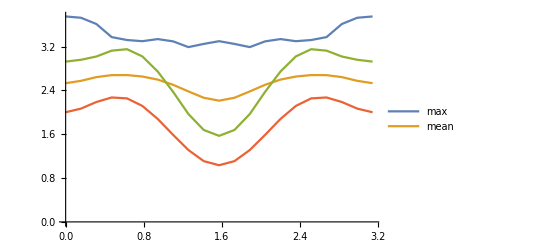

```mathematica
ListLinePlot[{kacrsnmax,kacrsnmean,rdnmax,rdmean},PlotLegends->{"max","mean"}]
```

```mathematica
ListLinePlot[Table[fibon[[n]],{n,1,6}]]
```

Part::partd: Part specification fibon⟦1⟧ is longer than depth of object.

Part::partd: Part specification fibon⟦2⟧ is longer than depth of object.

Part::partd: Part specification fibon⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

## dt = pi/16

#### 4+4 consecutive

#### data

```mathematica
rd16={-0.000000000000000000*10^+00,1.999999999999999778*10^+00,3.566474407432531635*10^+00,2.864929474810138377*10^+00,2.755013002877911177*10^+00,2.838271039832096498*10^+00,2.217443756428510770*10^+00,2.171435013325520025*10^+00,2.128821552943432671*10^+00,2.331125191574612732*10^+00,2.415085026709894223*10^+00,1.861704916377686647*10^+00,2.064793904825613868*10^+00,1.782932032933921995*10^+00,1.289308727637758167*10^+00,1.706946359679172298*10^+00,2.062699022481366828*10^+00,2.669482527733201493*10^+00,2.555601594996985249*10^+00,2.192952554407237464*10^+00,2.029593364389523202*10^+00,2.614690838615267410*10^+00,2.368900836885765138*10^+00,2.344083567818358915*10^+00,2.537716369486085810*10^+00,2.359962451217926471*10^+00,2.194234662462757335*10^+00,1.929941164947122534*10^+00,1.913352058760193097*10^+00,2.515452553080537612*10^+00,2.596159317328250449*10^+00,2.102704566198272840*10^+00,1.610729482567663240*10^+00,1.642562674340581230*10^+00,1.779743639898482943*10^+00,2.044132759650900688*10^+00,2.319735444415718995*10^+00,2.177135859216390301*10^+00,2.012473408553151710*10^+00,2.383335097568376248*10^+00,1.932148719491923572*10^+00,1.740834343449620292*10^+00,2.169645174711578584*10^+00,2.222286429549402698*10^+00,2.574113721033575164*10^+00,2.636611289209014775*10^+00,3.258018460553442797*10^+00,2.074867194726182529*10^+00,1.204185010213120410*10^+00,2.245193750592611615*10^+00,3.077774180321316333*10^+00,2.980784935062257279*10^+00,2.057295463147031711*10^+00,2.201594394566344093*10^+00,2.728438275626225540*10^+00,2.325836164352669044*10^+00,1.779680720477740730*10^+00,2.102792829149443321*10^+00,2.369453739222585398*10^+00,2.819058474464808839*10^+00,3.201219764591729966*10^+00,2.788030605846496535*10^+00,2.424003621219458893*10^+00,2.103770063792303358*10^+00,2.133357165144677658*10^+00,2.214473688272240004*10^+00,2.232163573278354907*10^+00,2.353351230700754471*10^+00,1.640443852248491652*10^+00,2.363907928618283361*10^+00,2.463325182417029247*10^+00,1.518775956843881003*10^+00,1.662638151331189196*10^+00,2.131164725154021333*10^+00,2.886203323181832481*10^+00,2.127555164355486639*10^+00,2.280711784302908551*10^+00,2.295204938147739071*10^+00,2.160186808876873421*10^+00,2.787635803469930895*10^+00,2.748045406280301250*10^+00,2.506743939293468948*10^+00,2.775451840773604850*10^+00,2.813317351148712842*10^+00,2.040497847325964287*10^+00,2.059485471187703531*10^+00,2.299136187021290745*10^+00,1.634612023577924678*10^+00,1.809251293054767284*10^+00,1.727643063209875152*10^+00,2.039740283962143685*10^+00,1.307032800673523898*10^+00,2.170524100928947320*10^+00,3.470585819496289304*10^+00,2.900873996962212154*10^+00,3.104416012103244249*10^+00,2.620784098335744439*10^+00,2.415711962959641301*10^+00,2.332450956214979776*10^+00,2.463417809915684487*10^+00,1.816630060807458369*10^+00,2.104264454522192906*10^+00,2.481176016204633239*10^+00,2.141417234741416209*10^+00,1.752355337316173323*10^+00,2.463276874638268499*10^+00,2.567339548859005838*10^+00,2.815312991672194620*10^+00,3.727772176128144377*10^+00,2.318021158640891421*10^+00,1.833737525807555446*10^+00,1.778970968661975682*10^+00,2.310082903504959262*10^+00,3.057199384112734286*10^+00,2.062307167468746094*10^+00,2.229211004329535228*10^+00,2.504978519416717564*10^+00,2.339734674044437579*10^+00,2.654734169421235634*10^+00,2.189883432274930097*10^+00,1.867058217289536026*10^+00,3.119377554146868459*10^+00,2.787503363733258688*10^+00,2.549752179092662274*10^+00,1.953206098116009759*10^+00,2.233295082700081480*10^+00,2.695300850127816172*10^+00,2.673247648083004968*10^+00,2.107293748880993967*10^+00,1.687924463738892378*10^+00,2.878164092507463412*10^+00,2.268577664847699182*10^+00,1.792986844470024321*10^+00,2.219726788711212428*10^+00,2.542957527201560097*10^+00,2.422970859546769606*10^+00,2.721925899907617463*10^+00,2.625810687034174418*10^+00,2.470389197185060226*10^+00,2.438796106016153598*10^+00,2.119947694131376625*10^+00,2.346067895697762751*10^+00,1.922608771334465949*10^+00,2.298152366923357448*10^+00,2.259440590916851566*10^+00,2.588543641824156083*10^+00,3.174008419072658960*10^+00,3.376083611047818511*10^+00,2.628851574250174128*10^+00,2.302088659734227161*10^+00,1.838882395272324555*10^+00,2.042068215825572963*10^+00,2.565883967843694879*10^+00,2.513841952170568828*10^+00,2.252890092550948076*10^+00,1.855832010020204592*10^+00,2.405820060613181433*10^+00,2.966652302066890012*10^+00,2.706867426628057682*10^+00,2.795250829246857194*10^+00,2.972318855071401700*10^+00,2.174083852145121121*10^+00,1.706638075195337390*10^+00,2.217646568014497888*10^+00,2.468125549272301100*10^+00,2.889096946040524028*10^+00,2.132424859971616016*10^+00,1.513892102197202272*10^+00,1.755583778407173945*10^+00,2.518330936804642484*10^+00,2.296719097985756797*10^+00,2.394460065958255335*10^+00,2.663484994940445105*10^+00,2.845382172873505588*10^+00,2.430375719767758014*10^+00,2.546343687907689723*10^+00,2.545915137630077929*10^+00,2.176654014631818068*10^+00,1.956013448116008302*10^+00,1.883021657188856945*10^+00,1.104212984139505860*10^+00,1.752999067528824728*10^+00,2.478622603260136170*10^+00,2.131536656803070251*10^+00,2.020476081772902610*10^+00,2.367255126762015216*10^+00,2.454431244203655993*10^+00,2.228826460508637641*10^+00,3.568076961840717320*10^+00,2.471725858803552889*10^+00,2.241071092241599949*10^+00,1.727341146037084663*10^+00,2.245645290590095211*10^+00,3.071633428959708922*10^+00,2.924024480866895814*10^+00,2.556054563874473384*10^+00,2.141141981685779072*10^+00,2.128086978285292918*10^+00,2.998126705748536125*10^+00,2.614021907419386892*10^+00,2.722912528242654327*10^-14,1.989665513936312635*10^+00,3.547968422588196891*10^+00,2.958067913517514747*10^+00,2.797708958152271386*10^+00,2.784758281307638583*10^+00,2.236428770069198269*10^+00,2.235493217576727254*10^+00,2.247385402068066806*10^+00,2.437383703866172091*10^+00,2.606530295799466934*10^+00,2.085101626965169430*10^+00,2.254279304995196576*10^+00,1.950131289963890291*10^+00,1.557903858790398166*10^+00,1.934770399044467570*10^+00,2.303456158862939418*10^+00,2.798347254700429332*10^+00,2.709529546208860218*10^+00,2.388291775433960762*10^+00,2.258152213973619205*10^+00,2.692711019652496152*10^+00,2.528666299888462365*10^+00,2.540302042330397914*10^+00,2.679358639873099968*10^+00,2.510442746641076806*10^+00,2.375569199523434705*10^+00,2.156409254050922097*10^+00,2.123436943986739767*10^+00,2.589389423776804033*10^+00,2.611964782392705686*10^+00,2.169218773365732211*10^+00,1.791931705819524545*10^+00,1.844272884524960521*10^+00,1.936618223573010278*10^+00,2.186674108316791099*10^+00,2.486417822849670500*10^+00,2.350887949235199947*10^+00,2.154449613987861945*10^+00,2.449617370620718049*10^+00,1.961271477870612401*10^+00,1.782128646883514911*10^+00,2.191164955469497855*10^+00,2.220310049721371470*10^+00,2.638187656114317825*10^+00,2.658056466973581777*10^+00,3.268892673942997096*10^+00,2.231635279401262384*10^+00,1.418663529649549115*10^+00,2.307736825755675625*10^+00,3.082504409609248874*10^+00,3.061642910078911761*10^+00,2.210939171367281020*10^+00,2.267426660971241237*10^+00,2.690735468243798945*10^+00,2.307160742354284366*10^+00,1.833546901397727247*10^+00,2.171889465072053049*10^+00,2.415276436213360522*10^+00,2.847249929254672018*10^+00,3.252516906483847947*10^+00,2.858473055689699560*10^+00,2.521315985285522920*10^+00,2.205300291003953195*10^+00,2.264934813107801315*10^+00,2.393501688275626815*10^+00,2.416339827651825090*10^+00,2.531310455242802071*10^+00,1.911676738401085984*10^+00,2.519106018673022085*10^+00,2.591150389930729325*10^+00,1.745039887574067805*10^+00,1.859526592236456555*10^+00,2.280646701968157330*10^+00,2.973392941600586870*10^+00,2.300601069479547789*10^+00,2.321481493539733876*10^+00,2.325939175724831998*10^+00,2.177078984371425996*10^+00,2.770947046922215495*10^+00,2.717411079503703419*10^+00,2.517567086824181732*10^+00,2.757062615452333887*10^+00,2.802520171303731544*10^+00,2.090326467449690639*10^+00,2.203648060386799390*10^+00,2.396341100558400328*10^+00,1.774505067841514627*10^+00,1.908285287906095196*10^+00,1.841567411279716460*10^+00,2.168202275931177425*10^+00,1.529274658471743153*10^+00,2.331573007419642352*10^+00,3.430500691300711669*10^+00,2.869168167130009994*10^+00,3.024244151949623483*10^+00,2.596463415827536370*10^+00,2.457418732544630835*10^+00,2.497994754408200180*10^+00,2.675873118373671922*10^+00,2.096410266136882417*10^+00,2.327952014141153381*10^+00,2.591386193563789409*10^+00,2.287414904078503675*10^+00,1.895354873487180791*10^+00,2.453353205007936744*10^+00,2.577123526204088577*10^+00,2.841647625648738629*10^+00,3.671074109299476973*10^+00,2.466991031200090223*10^+00,2.001427349455176863*10^+00,1.907367423226279390*10^+00,2.349870473686983097*10^+00,3.030042069801110127*10^+00,2.097697688095065516*10^+00,2.290098248333869435*10^+00,2.576034115204979269*10^+00,2.451670232798127458*10^+00,2.772861332789870570*10^+00,2.319530315984021929*10^+00,2.019192596345631863*10^+00,3.121583812761437038*10^+00,2.772280352787523494*10^+00,2.568041986248126296*10^+00,2.185117635616339982*10^+00,2.416866478529845264*10^+00,2.807120361665695896*10^+00,2.684133408845883917*10^+00,2.171172042992757234*10^+00,1.821774750238062568*10^+00,2.864461782267877510*10^+00,2.403987307811833229*10^+00,1.964821986489368788*10^+00,2.293140509111407876*10^+00,2.550761218936771435*10^+00,2.412432095643607610*10^+00,2.717400273030207813*10^+00,2.626816617838640511*10^+00,2.531413451021722771*10^+00,2.524075644334753399*10^+00,2.276017208792404212*10^+00,2.518795074056357386*10^+00,2.135853143773781770*10^+00,2.479649930176034189*10^+00,2.494362509732265920*10^+00,2.698832810909959079*10^+00,3.189096857092075687*10^+00,3.374467521228996958*10^+00,2.794230812782203088*10^+00,2.443123450155133103*10^+00,2.035436342768125684*10^+00,2.237095730825172435*10^+00,2.662977694977739063*10^+00,2.595484626814220430*10^+00,2.303241338096096769*10^+00,1.909786866674274997*10^+00,2.452407709799620417*10^+00,2.961037738565576394*10^+00,2.752831558083799202*10^+00,2.833057800390089476*10^+00,3.000898776627879183*10^+00,2.311448718839354211*10^+00,1.875521208734408418*10^+00,2.347283052773986078*10^+00,2.572626445797391082*10^+00,2.947758542109097490*10^+00,2.301348157844361531*10^+00,1.744726015217233250*10^+00,1.981868937545323561*10^+00,2.683226972864559912*10^+00,2.469478568584753564*10^+00,2.562186193324082151*10^+00,2.799549320089566695*10^+00,2.804308188962790105*10^+00,2.402736019430447012*10^+00,2.478890175154214504*10^+00,2.490621368062206464*10^+00,2.190897359492303575*10^+00,2.056643508339688342*10^+00,1.984513467283777644*10^+00,1.272696128296903817*10^+00,1.953911293369970270*10^+00,2.589581320588685287*10^+00,2.228413713407465302*10^+00,2.061879526157310405*10^+00,2.406568816206881234*10^+00,2.501390222093199167*10^+00,2.306057525903808081*10^+00,3.462066058497396792*10^+00,2.503309041690023662*10^+00,2.337975394491112802*10^+00,1.859676911487833983*10^+00,2.308094003150496398*10^+00,3.046184828378091236*10^+00,2.941964619589836794*10^+00,2.662265577642529024*10^+00,2.287722458925573576*10^+00,2.204655493919380760*10^+00,3.018154207554720969*10^+00,2.732550707152718861*10^+00,-9.610279511444755881*10^-16,1.959744107020122916*10^+00,3.495236611784322545*10^+00,3.150254602084694433*10^+00,2.931792036885397579*10^+00,2.666308902052327845*10^+00,2.265903252653724831*10^+00,2.392367334966869041*10^+00,2.475748344679444379*10^+00,2.662235622181169603*10^+00,2.835359322214246358*10^+00,2.443254274556163175*10^+00,2.489105304913847849*10^+00,2.172661573715676031*10^+00,1.979044597576143039*10^+00,2.350553271174093517*10^+00,2.691816205241860160*10^+00,2.898791781920224686*10^+00,2.919907545041823482*10^+00,2.685211014443729560*10^+00,2.620195462554688159*10^+00,2.801772548609325231*10^+00,2.716456848170900606*10^+00,2.741996631385686722*10^+00,2.820925522730347357*10^+00,2.762564998455806720*10^+00,2.671443665089141106*10^+00,2.554035875173578329*10^+00,2.479531246586207160*10^+00,2.695544969322333451*10^+00,2.618903287958128878*10^+00,2.256154563994784645*10^+00,2.146859742682004857*10^+00,2.189159573906521494*10^+00,2.196490918911327750*10^+00,2.403295634522491397*10^+00,2.733524168422969858*10^+00,2.621390924347112072*10^+00,2.420780683153217261*10^+00,2.578844066124714285*10^+00,2.059649231372876699*10^+00,1.909034025191129968*10^+00,2.247415595526168097*10^+00,2.253000020866025466*10^+00,2.729306250004365886*10^+00,2.727577330032668890*10^+00,3.280615687612238762*10^+00,2.472063735133898543*10^+00,1.801836644065371473*10^+00,2.392919645579595134*10^+00,3.021110196992269792*10^+00,3.110511559812610294*10^+00,2.421855178605616388*10^+00,2.305061701072555813*10^+00,2.565147556985135857*10^+00,2.225922570127660371*10^+00,1.932944240964688198*10^+00,2.325850486885387536*10^+00,2.494953555857723160*10^+00,2.914123668963805258*10^+00,3.307509311141864750*10^+00,2.924924412970556276*10^+00,2.629281762915654852*10^+00,2.372242045797611443*10^+00,2.483408670835448362*10^+00,2.690663164082292447*10^+00,2.702554220476584224*10^+00,2.870695535328090298*10^+00,2.413837099745888004*10^+00,2.772654338280825304*10^+00,2.839500729861385686*10^+00,2.112808970416857335*10^+00,2.166375018126989183*10^+00,2.504746063511589238*10^+00,3.067413438598827646*10^+00,2.578420150199476346*10^+00,2.420206107197613310*10^+00,2.389546199602617271*10^+00,2.209589902272857564*10^+00,2.757070819146005825*10^+00,2.634252197775338367*10^+00,2.517189866627901118*10^+00,2.746305481238055179*10^+00,2.759770006402895604*10^+00,2.197647240807183433*10^+00,2.397201579222366874*10^+00,2.532109073149756640*10^+00,2.002090712675897777*10^+00,2.074566716666160993*10^+00,2.108485380097334438*10^+00,2.445269643929266046*10^+00,1.933721190486641595*10^+00,2.590181679011845262*10^+00,3.302149747646497158*10^+00,2.752650455141168351*10^+00,2.780110548088460032*10^+00,2.503908305431845172*10^+00,2.523526960668726726*10^+00,2.804338934933758853*10^+00,3.002769811355325391*10^+00,2.586562908068285260*10^+00,2.713215010859879595*10^+00,2.779991842168426430*10^+00,2.541926931483986962*10^+00,2.185559931973251047*10^+00,2.432293399198210526*10^+00,2.560965595149187202*10^+00,2.862334730806598948*10^+00,3.513403524961244528*10^+00,2.746865278418239242*10^+00,2.328836100792537778*10^+00,2.200797223766377542*10^+00,2.450846518882086933*10^+00,2.984726764966693757*10^+00,2.187514182694307863*10^+00,2.378281523107222739*10^+00,2.633578806256865690*10^+00,2.608825518143726541*10^+00,2.888463893892613044*10^+00,2.501310980808954199*10^+00,2.278785372803292741*10^+00,3.074879699407669698*10^+00,2.730295175001749897*10^+00,2.601276121115795537*10^+00,2.599906268852695934*10^+00,2.717974390524514838*10^+00,2.984961862159364543*10^+00,2.760543455461792473*10^+00,2.325186523609685363*10^+00,2.106094326038496334*10^+00,2.870770068160554800*10^+00,2.615920284805961948*10^+00,2.277668723096065939*10^+00,2.458459869264536746*10^+00,2.591249083117437735*10^+00,2.375021545341681861*10^+00,2.653233591589857276*10^+00,2.605770870853346022*10^+00,2.640936470251116219*10^+00,2.715765999094576610*10^+00,2.544024629543795157*10^+00,2.764620681138054703*10^+00,2.449050423112580255*10^+00,2.757888156642394506*10^+00,2.815140154382698601*10^+00,2.894991187623388917*10^+00,3.253470873333041080*10^+00,3.348859409838298440*10^+00,3.011525327550401254*10^+00,2.632395138352598085*10^+00,2.368614423042372685*10^+00,2.613665721278128018*10^+00,2.823459979037406864*10^+00,2.795419994037261713*10^+00,2.395436642576686648*10^+00,2.051362632024921862*10^+00,2.515144284896594140*10^+00,2.964083528685519831*10^+00,2.812421347042747044*10^+00,2.858668109536606217*10^+00,3.037514434641625627*10^+00,2.575294489741986492*10^+00,2.209592087144160111*10^+00,2.535151609917137172*10^+00,2.673943966746063605*10^+00,3.024795213621528589*10^+00,2.528276300411053334*10^+00,2.140308832539761230*10^+00,2.400854178740165601*10^+00,2.903257854455342901*10^+00,2.711323162930415975*10^+00,2.786222594924905760*10^+00,2.922979124876083912*10^+00,2.710960814171775368*10^+00,2.337018732317789116*10^+00,2.345886175796670692*10^+00,2.370245452647215423*10^+00,2.222498402691206021*10^+00,2.285486446414607631*10^+00,2.158833167923149166*10^+00,1.590278394772639325*10^+00,2.299699439680864099*10^+00,2.783873582498912480*10^+00,2.402001657820026281*10^+00,2.146200634163226262*10^+00,2.469653498315694140*10^+00,2.558515073330809741*10^+00,2.363343638058560181*10^+00,3.210765266922745553*10^+00,2.540231466524206283*10^+00,2.508671121409150828*10^+00,2.179461964509398886*10^+00,2.439967373766116943*10^+00,3.012847330656938105*10^+00,2.994554164240567751*10^+00,2.895684286249461614*10^+00,2.589956551445563804*10^+00,2.331644619549965824*10^+00,3.008705708902705389*10^+00,2.906577559252143672*10^+00,9.610279511444749964*10^-16,1.913351667118160737*10^+00,3.415489142817916601*10^+00,3.282065197303480009*10^+00,3.003495496699434053*10^+00,2.500685747590501329*10^+00,2.291124443822572854*10^+00,2.544240580596627943*10^+00,2.707908134523487220*10^+00,2.844742949205553373*10^+00,2.972181070752569099*10^+00,2.723085914592148882*10^+00,2.605217421947927381*10^+00,2.264099364133736358*10^+00,2.271075884141325218*10^+00,2.684484185880005480*10^+00,3.004333290140439594*10^+00,2.861178670391721024*10^+00,3.000681789773449015*10^+00,2.876576712469024244*10^+00,2.900145805172881897*10^+00,2.812043271383991350*10^+00,2.745372149541330575*10^+00,2.714244297551075213*10^+00,2.775273573465214749*10^+00,2.964699399072481256*10^+00,2.913205960759030155*10^+00,2.897128703687425144*10^+00,2.726357214193563472*10^+00,2.705227592887025079*10^+00,2.585897697313847665*10^+00,2.364915924554376492*10^+00,2.452104703609556235*10^+00,2.463160568156796515*10^+00,2.404539332148866393*10^+00,2.596309624954463047*10^+00,2.898402613903230840*10^+00,2.780114765098877783*10^+00,2.637987651785977938*10^+00,2.708752694856364052*10^+00,2.220495105699449745*10^+00,2.077658774309548040*10^+00,2.258657755629794650*10^+00,2.281720408462855065*10^+00,2.788488015028944389*10^+00,2.763984602726942352*10^+00,3.267670227228907986*10^+00,2.660368630040787608*10^+00,2.146793914823602378*10^+00,2.417599143184986588*10^+00,2.856854215404643682*10^+00,2.993344133182173739*10^+00,2.517234226659269325*10^+00,2.248683572736838610*10^+00,2.308143365053561880*10^+00,2.033480350818256621*10^+00,1.954792996176116127*10^+00,2.445708399952619239*10^+00,2.591670888128242645*10^+00,2.957687477520889452*10^+00,3.260431782112639620*10^+00,2.889717187011588084*10^+00,2.612372472309017368*10^+00,2.468325624539328800*10^+00,2.608757057234045718*10^+00,2.912069972107617755*10^+00,2.923130749902830061*10^+00,3.113649450622467452*10^+00,2.823963690087154976*10^+00,2.943840349335220097*10^+00,3.050689479554133055*10^+00,2.439588799786680529*10^+00,2.373243109938513840*10^+00,2.642415095073801901*10^+00,3.086209838678154238*10^+00,2.861060736227241552*10^+00,2.575608184522979904*10^+00,2.444225695143704691*10^+00,2.231879915694722882*10^+00,2.735305516053326169*10^+00,2.563208480480211993*10^+00,2.521327858540893807*10^+00,2.706551926515980533*10^+00,2.721373774629578079*10^+00,2.327649093046301854*10^+00,2.542741782490041125*10^+00,2.594653109194865692*10^+00,2.214491668807612168*10^+00,2.259599530466831929*10^+00,2.342640463096415271*10^+00,2.712022383214289789*10^+00,2.311165609492926265*10^+00,2.785805209575032748*10^+00,3.120287368064929900*10^+00,2.552743356949219944*10^+00,2.405855774268566893*10^+00,2.324934740584560622*10^+00,2.552373907012408960*10^+00,3.031866736005683016*10^+00,3.229431485727997764*10^+00,2.974564839136066396*10^+00,2.941524998024851900*10^+00,2.862990538986714295*10^+00,2.701865997815203091*10^+00,2.457128005455775366*10^+00,2.462513726248839241*10^+00,2.519298162857676271*10^+00,2.813845791820746456*10^+00,3.292690794131218901*10^+00,2.928513939347781481*10^+00,2.580613366676385745*10^+00,2.470123302338451232*10^+00,2.564984371856087186*10^+00,2.983775405306229089*10^+00,2.323214932805551136*10^+00,2.423010863953347638*10^+00,2.590791171357052836*10^+00,2.605700687580793762*10^+00,2.821854885763088294*10^+00,2.623985802138304901*10^+00,2.487749677713658514*10^+00,2.959128645422416604*10^+00,2.637432421722287312*10^+00,2.615279632460904224*10^+00,2.939661336132042280*10^+00,2.885204594903976183*10^+00,3.102870565869266795*10^+00,2.877770108538974636*10^+00,2.457030974197602191*10^+00,2.375914716079921440*10^+00,2.815512451954343298*10^+00,2.729966992022029970*10^+00,2.492749196784547205*10^+00,2.601111747643213068*10^+00,2.614797334847354104*10^+00,2.306726629600526213*10^+00,2.504200169259815034*10^+00,2.586458466487767449*10^+00,2.779433466305789580*10^+00,2.858736177243625498*10^+00,2.746918274367603718*10^+00,2.904707568958552422*10^+00,2.636797250417485472*10^+00,2.893954921555979887*10^+00,2.967670790283786442*10^+00,3.034219982683974859*10^+00,3.277896260009977247*10^+00,3.266228631648285585*10^+00,3.080701932619938965*10^+00,2.724994001935430177*10^+00,2.613047961671139507*10^+00,2.928538688727263750*10^+00,2.910527287743555291*10^+00,2.946786454367427588*10^+00,2.467133576008624818*10^+00,2.169679216331846128*10^+00,2.574030070737156617*10^+00,2.961764147719130769*10^+00,2.809684612661475178*10^+00,2.770578205247620218*10^+00,2.976817760255755729*10^+00,2.734085866557306232*10^+00,2.511740284498899634*10^+00,2.625214991087346572*10^+00,2.631379690321429710*10^+00,3.038642513340726214*10^+00,2.639944505026691868*10^+00,2.438323570296009102*10^+00,2.735666180542800419*10^+00,3.012964794803167035*10^+00,2.852015530454103498*10^+00,2.860216339492466009*10^+00,2.879491123613623582*10^+00,2.597944661957606982*10^+00,2.241537062110137146*10^+00,2.224846154565695677*10^+00,2.305948068152325003*10^+00,2.319306734172367435*10^+00,2.499858651179568181*10^+00,2.279140651371917237*10^+00,1.854158754000052367*10^+00,2.574491471881218185*10^+00,2.937662264599563144*10^+00,2.601942611771739688*10^+00,2.316520278271134714*10^+00,2.543442917767446243*10^+00,2.491669838547887483*10^+00,2.319817774618273987*10^+00,2.912439731195017867*10^+00,2.545432354388514007*10^+00,2.706466871634655380*10^+00,2.559449024636148984*10^+00,2.612895202319603705*10^+00,2.977534806594956507*10^+00,3.072118676992394271*10^+00,3.103504647894092194*10^+00,2.828388728712673217*10^+00,2.422470618235633033*10^+00,2.918479477653937337*10^+00,2.907608405891923375*10^+00,4.805139755722374982*10^-16,1.855267229865799727*10^+00,3.317784672913314026*10^+00,3.307697246040516958*10^+00,2.991263697107698238*10^+00,2.383608582413415888*10^+00,2.314658492539905410*10^+00,2.683498760888524792*10^+00,2.887597688688053665*10^+00,2.945460985111618690*10^+00,3.019221060574600379*10^+00,2.896882893031671902*10^+00,2.604035362275999077*10^+00,2.221308671964966841*10^+00,2.359449602002772650*10^+00,2.857949242990072136*10^+00,3.176358207092824681*10^+00,2.736401670337650582*10^+00,2.929021158068020991*10^+00,2.907692707795630493*10^+00,2.982354924689339715*10^+00,2.741905376686078810*10^+00,2.638368345370664780*10^+00,2.475649013949243304*10^+00,2.567171374070079004*10^+00,3.109163652351613294*10^+00,3.079937520853675448*10^+00,3.055226199719872415*10^+00,2.798100908941125287*10^+00,2.665352401327868659*10^+00,2.541489482332115024*10^+00,2.499862378776095184*10^+00,2.661537338852055345*10^+00,2.646286248337148539*10^+00,2.568843240736267575*10^+00,2.778600790844190538*10^+00,2.999188916432308449*10^+00,2.782493303418412722*10^+00,2.742319483186174800*10^+00,2.824987548290887052*10^+00,2.439387678638732737*10^+00,2.268656811442992360*10^+00,2.238760956117085144*10^+00,2.275454467568142292*10^+00,2.811767660358773568*10^+00,2.761978725408965385*10^+00,3.222952280246936585*10^+00,2.745788178320167194*10^+00,2.379373998957383662*10^+00,2.403226263651088157*10^+00,2.638199172751839683*10^+00,2.809300799386485359*10^+00,2.470482798519105128*10^+00,2.126822277904727443*10^+00,2.060287212649599464*10^+00,1.757618161708156990*10^+00,1.848038257748077395*10^+00,2.473381325266978070*10^+00,2.722163479476971570*10^+00,2.948516344138104373*10^+00,3.123421873456666553*10^+00,2.855553855783717232*10^+00,2.595837837546167481*10^+00,2.496115378850091382*10^+00,2.600782965796867963*10^+00,3.013165523907937793*10^+00,3.025933843661960942*10^+00,3.169521200540486028*10^+00,3.038302095985716544*10^+00,3.004519230590849688*10^+00,3.176947604610118603*10^+00,2.735828412036000135*10^+00,2.496658781381791758*10^+00,2.674811836907224905*10^+00,3.070570618473031033*10^+00,3.101848983543400884*10^+00,2.717422681394230377*10^+00,2.461498875489000593*10^+00,2.213210307955405298*10^+00,2.684228529941212749*10^+00,2.495644036540211275*10^+00,2.496677420144145287*10^+00,2.636591432330012807*10^+00,2.789442901472188208*10^+00,2.500635061685826166*10^+00,2.647283463797884817*10^+00,2.615555422880758485*10^+00,2.382436833864117531*10^+00,2.461930643602564750*10^+00,2.486344826046852141*10^+00,2.923953799595404579*10^+00,2.613613109537091361*10^+00,2.885893325301674750*10^+00,3.002439312250868575*10^+00,2.444710085315237702*10^+00,2.079582011150752585*10^+00,2.135667981327619813*10^+00,2.515999643826814847*10^+00,3.121305375053562425*10^+00,3.289835629454478383*10^+00,3.145068599099514639*10^+00,2.943226763996500850*10^+00,2.776110693474195035*10^+00,2.709578828149322938*10^+00,2.665343395722290953*10^+00,2.527321830045972995*10^+00,2.438040040148003129*10^+00,2.706509866409644083*10^+00,3.060068033169169865*10^+00,2.905054572350217690*10^+00,2.643920645882588349*10^+00,2.595838222274645446*10^+00,2.607780571214098675*10^+00,3.021916855412247749*10^+00,2.472255394244616600*10^+00,2.455079562461149667*10^+00,2.455884337826180097*10^+00,2.433690920839636007*10^+00,2.594149340463665965*10^+00,2.674668786450210334*10^+00,2.672124062856997551*10^+00,2.811536059394826204*10^+00,2.536868614343385175*10^+00,2.635427598385935433*10^+00,3.132987877252149556*10^+00,2.905757982971477915*10^+00,3.157731185963049914*10^+00,2.988399460165843013*10^+00,2.553707655142095412*10^+00,2.566922012335779435*10^+00,2.694781282360354968*10^+00,2.723103672542747766*10^+00,2.564038560471055828*10^+00,2.637011074622030105*10^+00,2.628498357387869078*10^+00,2.227941328903024321*10^+00,2.344087640583680798*10^+00,2.579225780388818112*10^+00,2.919738527766285507*10^+00,2.976513240311380759*10^+00,2.871334665799968988*10^+00,2.921905990730249147*10^+00,2.681775376210360218*10^+00,2.853081397689455123*10^+00,2.932713467137508800*10^+00,3.069878769738415336*10^+00,3.249941486747992325*10^+00,3.141868287330011889*10^+00,3.004255545658742754*10^+00,2.793508341767941161*10^+00,2.800498077425328081*10^+00,3.166971293638259688*10^+00,3.046363822398300947*10^+00,2.980420397958617684*10^+00,2.572251968942326883*10^+00,2.376984628407943667*10^+00,2.695464870176166539*10^+00,3.024443677938900343*10^+00,2.801946095139908000*10^+00,2.637237518737840070*10^+00,2.848507682468701230*10^+00,2.776928914178479868*10^+00,2.720232486927940840*10^+00,2.665957585232663796*10^+00,2.576325168309496760*10^+00,3.008521580295135944*10^+00,2.614402949740092019*10^+00,2.535820421507011702*10^+00,2.893951738600127221*10^+00,3.037920927868022591*10^+00,2.877630490329691426*10^+00,2.765577984040766601*10^+00,2.696804098434829378*10^+00,2.468684346347270520*10^+00,2.136400000082008255*10^+00,2.155106560154205653*10^+00,2.307561901501854251*10^+00,2.488792244627475281*10^+00,2.684607615071533004*10^+00,2.379133437888818925*10^+00,2.060371758180151058*10^+00,2.745405661667251529*10^+00,3.057425630841502429*10^+00,2.822091113708291132*10^+00,2.588917552815912515*10^+00,2.573265619581143415*10^+00,2.343310996750361586*10^+00,2.234027804028994701*10^+00,2.675167159507184866*10^+00,2.537208464784175721*10^+00,2.842912906461766198*10^+00,2.874262763860431669*10^+00,2.830050673964766617*10^+00,2.912038348702103541*10^+00,3.123621632967963357*10^+00,3.213282490134348190*10^+00,2.950869645549508924*10^+00,2.460244317879900944*10^+00,2.782181998992293348*10^+00,2.727462086955312781*10^+00,3.203426503814917641*10^-16,1.791378800394229032*10^+00,3.210908538316554761*10^+00,3.223596370127034483*10^+00,2.926870117247332814*10^+00,2.436737517671334619*10^+00,2.388389195596185566*10^+00,2.825824864773450962*10^+00,3.013350445814690026*10^+00,2.965910635824599240*10^+00,3.018567674928605449*10^+00,3.000018617420276090*10^+00,2.587029605433475599*10^+00,2.200747554437676889*10^+00,2.312311805977589785*10^+00,2.907732632342485246*10^+00,3.237972800396311968*10^+00,2.730836472426218631*10^+00,2.777535003508242895*10^+00,2.817868248876271853*10^+00,2.906991218027376256*10^+00,2.631544834840167102*10^+00,2.506244381246395037*10^+00,2.227723828194846156*10^+00,2.342852833757909981*10^+00,3.154423629499689685*10^+00,3.179899979577765823*10^+00,3.053627946963326512*10^+00,2.770206893866641540*10^+00,2.711801320496898260*10^+00,2.558453343973709604*10^+00,2.709665361093479330*10^+00,2.824128044612915112*10^+00,2.756769013372699639*10^+00,2.707201853905727873*10^+00,2.980333390437312158*10^+00,3.062819388437621804*10^+00,2.730280374102634244*10^+00,2.803299312559821566*10^+00,2.917403778884146259*10^+00,2.677586953788534618*10^+00,2.464369662522695403*10^+00,2.216425077317462744*10^+00,2.238686002686381293*10^+00,2.805308592696552861*10^+00,2.776444939479396190*10^+00,3.103082161587178867*10^+00,2.741638655308474615*10^+00,2.486387101715845205*10^+00,2.391192212939858841*10^+00,2.484478004231288395*10^+00,2.665201201056571989*10^+00,2.400779631924234714*10^+00,2.055890176752843690*10^+00,1.963533977552527343*10^+00,1.546834766985708542*10^+00,1.692419611815314084*10^+00,2.432107787662495468*10^+00,2.851920217341998853*10^+00,2.921032479381891367*10^+00,2.983575559301950619*10^+00,2.978572134637648361*10^+00,2.685709268287501228*10^+00,2.473862788228369247*10^+00,2.564993776707160666*10^+00,3.040093240032927024*10^+00,3.078106034350473585*10^+00,3.118112600256134126*10^+00,3.084116002159122072*10^+00,3.012942377673905714*10^+00,3.240633998342579591*10^+00,2.952092486867510690*10^+00,2.624739321053021879*10^+00,2.691518648556074034*10^+00,3.042068861365374577*10^+00,3.272996485426997282*10^+00,2.812300470714841794*10^+00,2.418558887649256750*10^+00,2.144222233388782151*10^+00,2.587202420269246517*10^+00,2.445913859455922434*10^+00,2.482740829877887023*10^+00,2.616949987046333082*10^+00,2.861936010953477716*10^+00,2.658771209340574426*10^+00,2.761133660255600475*10^+00,2.662539621410676016*10^+00,2.559066327975801691*10^+00,2.679098310289823370*10^+00,2.576440939969542931*10^+00,3.082095336142984365*10^+00,2.815499074751373509*10^+00,2.940330602780074631*10^+00,3.044398694732855404*10^+00,2.547619714223857912*10^+00,2.012539955041409367*10^+00,2.092374598864282564*10^+00,2.469978083210955688*10^+00,3.125902701127566630*10^+00,3.248923441057180117*10^+00,3.137786026812559026*10^+00,2.854830068563358303*10^+00,2.623171674187738667*10^+00,2.642960737176181851*10^+00,2.784085159304492407*10^+00,2.617036575552053268*10^+00,2.383138055296638580*10^+00,2.605224960476995921*10^+00,2.831601424620116880*10^+00,2.667258065936069400*10^+00,2.523710511634731368*10^+00,2.542112542264755692*10^+00,2.540298367648514688*10^+00,3.076003487094458588*10^+00,2.653752287783585295*10^+00,2.537716014547409138*10^+00,2.352954715668458263*10^+00,2.236391467563194624*10^+00,2.325988101497087790*10^+00,2.736810139003846842*10^+00,2.844287002200446057*10^+00,2.688482387303000376*10^+00,2.454946705752010239*10^+00,2.685578556770578551*10^+00,3.179221739004537195*10^+00,2.873576820808012577*10^+00,3.192951358582900134*10^+00,3.078848394386994869*10^+00,2.700605090272153674*10^+00,2.675530760614518222*10^+00,2.612375189901011474*10^+00,2.660972241693231322*10^+00,2.555592152911556170*10^+00,2.641630750959108376*10^+00,2.652486720570572665*10^+00,2.181146415215509560*10^+00,2.263109124257363103*10^+00,2.612971103512124582*10^+00,3.030833684362222336*10^+00,3.077754879253633558*10^+00,2.934732273799131708*10^+00,2.881377098216110877*10^+00,2.638585762543539381*10^+00,2.716397496299265413*10^+00,2.781288634523716219*10^+00,3.015422492858417236*10^+00,3.181410776358974069*10^+00,3.003484597066961470*10^+00,2.890030031008486766*10^+00,2.861169771694199504*10^+00,2.981536028187008913*10^+00,3.363067313527472457*10^+00,3.299635141935306493*10^+00,2.898016850105376463*10^+00,2.696909005961053207*10^+00,2.643508459171000524*10^+00,2.826026628857904566*10^+00,3.123823935338407853*10^+00,2.854238368536607062*10^+00,2.594216807293829419*10^+00,2.770007804492347958*10^+00,2.752608008929433581*10^+00,2.851197628676428231*10^+00,2.736219305896363529*10^+00,2.599236924535129667*10^+00,2.995048018222902009*10^+00,2.499236085736058044*10^+00,2.453350115111675223*10^+00,2.927586740007947164*10^+00,3.056128717340872214*10^+00,2.837712208139349990*10^+00,2.629919447427176316*10^+00,2.507159046300142080*10^+00,2.359282714530440028*10^+00,2.124068677808701011*10^+00,2.188933603879032130*10^+00,2.405771936938048139*10^+00,2.683577477694295332*10^+00,2.828026812635099141*10^+00,2.519573627397694970*10^+00,2.281227569951910894*10^+00,2.832786039147316970*10^+00,3.185659241188245616*10^+00,3.069167338159475733*10^+00,2.909614092873689106*10^+00,2.597707544040667393*10^+00,2.228822560291091825*10^+00,2.199927922142282721*10^+00,2.575008858104301801*10^+00,2.555512913021707355*10^+00,2.922208358891715818*10^+00,3.073162698772075707*10^+00,3.039063387195958477*10^+00,2.862947679242171972*10^+00,3.067122669524188883*10^+00,3.222916901324710537*10^+00,2.995341740455419899*10^+00,2.523515373603479439*10^+00,2.646785469298158500*10^+00,2.433798252642962012*10^+00,-9.610279511444755881*10^-16,1.728029267274305392*10^+00,3.103013626818908133*10^+00,3.081780606739900286*10^+00,2.854110428261539933*10^+00,2.601173052235179473*10^+00,2.512114955889679813*10^+00,2.926524079138370649*10^+00,3.091070576174914653*10^+00,2.908781005126982677*10^+00,2.959141168132614741*10^+00,3.043146042102802706*10^+00,2.617820761437764876*10^+00,2.289308517060367087*10^+00,2.256096093912040690*10^+00,2.882642779885100648*10^+00,3.219646858470842421*10^+00,2.779422488689935911*10^+00,2.641281028138634301*10^+00,2.677379835256359364*10^+00,2.685177963555227976*10^+00,2.538357622437645844*10^+00,2.467185904231564475*10^+00,2.091094634878276626*10^+00,2.202665067622648909*10^+00,3.169192027393878064*10^+00,3.254137555720970632*10^+00,2.983484144886162870*10^+00,2.766422109888273528*10^+00,2.853828930645610384*10^+00,2.617609373579680376*10^+00,2.921621790909137761*10^+00,2.999687147853227209*10^+00,2.811898810217813516*10^+00,2.811477940218551907*10^+00,3.147153741152955764*10^+00,3.079810765049774357*10^+00,2.716077953931784528*10^+00,2.859608670515834561*10^+00,2.978727026074301065*10^+00,2.890715881052635439*10^+00,2.649062941051164799*10^+00,2.279060592385338424*10^+00,2.193614928069501424*10^+00,2.792820494043998902*10^+00,2.727504674552939434*10^+00,2.903531113251341278*10^+00,2.657777008511477135*10^+00,2.474444286059400699*10^+00,2.386689394432734090*10^+00,2.473169957352079784*10^+00,2.682831967127467188*10^+00,2.372380800859997141*10^+00,2.108945841707583924*10^+00,2.050882055107683399*10^+00,1.506306988149330950*10^+00,1.629057228357433607*10^+00,2.346204994228117791*10^+00,2.942810620144907574*10^+00,2.861177023039986445*10^+00,2.867931087995113426*10^+00,3.138246524701894469*10^+00,2.889285391686625459*10^+00,2.458128151139657103*10^+00,2.558480616521444873*10^+00,3.062129309796021825*10^+00,3.122426548912895505*10^+00,3.048499469943749318*10^+00,3.059767692032635100*10^+00,3.012862850380275237*10^+00,3.260128517271642767*10^+00,3.092475695738393426*10^+00,2.747585711738395275*10^+00,2.707895185125623438*10^+00,3.036045168143295836*10^+00,3.373231309912296805*10^+00,2.814143008178630723*10^+00,2.324534620839045829*10^+00,2.080693351700994231*10^+00,2.486913685323481449*10^+00,2.388372035050284836*10^+00,2.461742321256181754*10^+00,2.660440700362823208*10^+00,2.906225862265595428*10^+00,2.744803695235951579*10^+00,2.817617193987623114*10^+00,2.745724755315129162*10^+00,2.734837829506075124*10^+00,2.840207581733227293*10^+00,2.627802526922607296*10^+00,3.161926612702287365*10^+00,2.944411646242766967*10^+00,2.974840810777020117*10^+00,3.203887894033115025*10^+00,2.795125584748126890*10^+00,2.176046487676246866*10^+00,2.236242895486581173*10^+00,2.451316434182588821*10^+00,3.106325151935809714*10^+00,3.179090620279121371*10^+00,3.078735806617508342*10^+00,2.810220951500850717*10^+00,2.520193997173454381*10^+00,2.584964841746826281*10^+00,2.798543480560991004*10^+00,2.672965506142563452*10^+00,2.413373581865467354*10^+00,2.544219636026628262*10^+00,2.642815458599196532*10^+00,2.303045748872043497*10^+00,2.297002460687616487*10^+00,2.356571969320874871*10^+00,2.362116830777107879*10^+00,3.093148415421707931*10^+00,2.914627312226184763*10^+00,2.722446174181717637*10^+00,2.384403232101108827*10^+00,2.156603721994511336*10^+00,2.198789053573555474*10^+00,2.812554808853272359*10^+00,2.989102219015442152*10^+00,2.615484492083237189*10^+00,2.414200940601152201*10^+00,2.725057183374409053*10^+00,3.107150866032078795*10^+00,2.865718405801930935*10^+00,3.222370593854531950*10^+00,3.127133758761025728*10^+00,2.890854037742262683*10^+00,2.767007625426747719*10^+00,2.660978513970187365*10^+00,2.655602421270178759*10^+00,2.576187021959726930*10^+00,2.662281273951684568*10^+00,2.718269364881812145*10^+00,2.220454538648593434*10^+00,2.296584807437842102*10^+00,2.675321687824222749*10^+00,3.086287917232655609*10^+00,3.097243905247853313*10^+00,2.960292830628885596*10^+00,2.849501715293320192*10^+00,2.616139431764782142*10^+00,2.580263486299921638*10^+00,2.614018300614914470*10^+00,2.910659631085998456*10^+00,3.086319991888423431*10^+00,2.868652403955028518*10^+00,2.780666687160195494*10^+00,2.942980207807351256*10^+00,3.114464403339386678*10^+00,3.497502052008203854*10^+00,3.502967005907737352*10^+00,2.749067193130797726*10^+00,2.762948952944326297*10^+00,2.891027901729479765*10^+00,2.985895778357586572*10^+00,3.198736269119279108*10^+00,2.929404315925008717*10^+00,2.676295374654832138*10^+00,2.785168357940639439*10^+00,2.695973212742007963*10^+00,2.873611490606337249*10^+00,2.806803131330634749*10^+00,2.702892720082367362*10^+00,3.014024455098672117*10^+00,2.409629100235374022*10^+00,2.316186736808451219*10^+00,2.894822470434938566*10^+00,3.109801462018489726*10^+00,2.832700424617698776*10^+00,2.599730118304325988*10^+00,2.421901125824914125*10^+00,2.327636834839001967*10^+00,2.181382966343993424*10^+00,2.280894096874898302*10^+00,2.496766318182285449*10^+00,2.874845302395658386*10^+00,2.908125888537184345*10^+00,2.692224069782344742*10^+00,2.527413474907228341*10^+00,2.897825577897462423*10^+00,3.270176756083319258*10^+00,3.273915507025536797*10^+00,3.101267926589837298*10^+00,2.609475012656283344*10^+00,2.194030092376931140*10^+00,2.286197167734235869*10^+00,2.614428421065452479*10^+00,2.600466785553744664*10^+00,2.945038689189696246*10^+00,3.113906163850068687*10^+00,3.190036006034388194*10^+00,2.890152950683050559*10^+00,2.964698523285867804*10^+00,3.160427660382761239*10^+00,2.995182892174246714*10^+00,2.654147359930295824*10^+00,2.562968856666879347*10^+00,2.168032792751832805*10^+00,-3.203426503814917641*10^-16,1.671356217449647907*10^+00,3.002677150067331269*10^+00,2.931926517360803341*10^+00,2.805517389661790872*10^+00,2.780573923062904740*10^+00,2.558988682560013217*10^+00,2.957116788725964618*10^+00,3.088359895306139524*10^+00,2.790179143653297444*10^+00,2.808656891639140341*10^+00,2.989718153519713262*10^+00,2.700892889470937419*10^+00,2.419739845213763285*10^+00,2.258654525515337852*10^+00,2.839477175346818427*10^+00,3.162774120683523815*10^+00,2.810144852331054821*10^+00,2.544912238104971358*10^+00,2.501975535152355157*10^+00,2.422723161325124330*10^+00,2.495774334894087509*10^+00,2.509257437000262048*10^+00,2.093175103247551405*10^+00,2.164022783844524067*10^+00,3.135430892836716055*10^+00,3.291435976119124529*10^+00,2.886782866144998572*10^+00,2.758165652753861607*10^+00,3.016342409945634628*10^+00,2.668984712026087891*10^+00,3.060424040503807674*10^+00,3.162743965496680243*10^+00,2.837504171649720242*10^+00,2.862075865013051335*10^+00,3.239651106433084848*10^+00,3.063529820349521149*10^+00,2.725271032013248274*10^+00,2.913126070370473997*10^+00,3.014409499984389118*10^+00,3.050345376185743085*10^+00,2.808083735305250794*10^+00,2.420644518257148547*10^+00,2.149627350137051529*10^+00,2.718181098383016803*10^+00,2.601474164685963153*10^+00,2.695149297351823847*10^+00,2.487209592087275212*10^+00,2.418364617986737297*10^+00,2.388030968195032244*10^+00,2.565906379051481778*10^+00,2.783779894459654347*10^+00,2.399817016650151569*10^+00,2.241651215669968611*10^+00,2.210122520700695148*10^+00,1.653904056414922330*10^+00,1.666153774789645992*10^+00,2.208217960464512686*10^+00,2.934252324162563319*10^+00,2.746933036525606386*10^+00,2.778804774550333256*10^+00,3.254572640935360806*10^+00,3.040076593951167805*10^+00,2.438354712972304661*10^+00,2.568444288616298365*10^+00,3.088336092914949926*10^+00,3.193763053562690857*10^+00,3.007284207279176336*10^+00,3.026594716112908756*10^+00,3.011385596454904778*10^+00,3.241108342156706179*10^+00,3.144194133322176565*10^+00,2.843773467258221110*10^+00,2.736202358873761842*10^+00,3.082610026996773556*10^+00,3.418598898524470631*10^+00,2.761345337413627199*10^+00,2.225288288162560413*10^+00,2.061390822841441484*10^+00,2.406862393570673220*10^+00,2.314972705587708290*10^+00,2.462528651505987654*10^+00,2.720528593154972086*10^+00,2.872929275584591657*10^+00,2.734946851401844903*10^+00,2.822494975617348523*10^+00,2.796408051941178918*10^+00,2.852398565507088701*10^+00,2.888315311167127142*10^+00,2.625143050876335149*10^+00,3.160096093518572680*10^+00,2.989571980575246091*10^+00,2.998201754048941403*10^+00,3.369863126134098774*10^+00,3.006992041528401494*10^+00,2.318363112968478301*10^+00,2.384722185688828766*10^+00,2.431010428759353026*10^+00,3.087768235095088798*10^+00,3.116805882587536214*10^+00,3.050520095584672298*10^+00,2.855398427279997264*10^+00,2.561997239993305087*10^+00,2.604533753147456387*10^+00,2.756658355510674063*10^+00,2.676371650753959219*10^+00,2.491081038574392448*10^+00,2.512084275634900443*10^+00,2.437006158826638291*10^+00,1.982070553502602639*10^+00,2.075656294895856568*10^+00,2.124340180938365297*10^+00,2.162005491761139986*10^+00,3.087935368430802185*10^+00,3.187436907352762638*10^+00,2.955011447970136373*10^+00,2.558567116176110545*10^+00,2.247306562292935794*10^+00,2.214452177143150013*10^+00,2.874149867063068076*10^+00,3.074694496007367661*10^+00,2.572355752119407146*10^+00,2.362812468382096132*10^+00,2.682962124043310137*10^+00,2.933333783750056600*10^+00,2.911025130367686842*10^+00,3.220707430715783914*10^+00,3.114890162688907171*10^+00,3.005076093703311191*10^+00,2.815105406084169815*10^+00,2.804267559385551056*10^+00,2.658172041863027246*10^+00,2.625416247049338736*10^+00,2.705270518190831641*10^+00,2.822454145322169428*10^+00,2.302035920555327131*10^+00,2.400122223033920754*10^+00,2.736848277852936384*10^+00,3.086553056640640502*10^+00,3.047323788189684635*10^+00,2.952078560516883776*10^+00,2.875106007721447199*10^+00,2.678178360807695668*10^+00,2.497206605707042115*10^+00,2.511236705839269945*10^+00,2.820636676645375207*10^+00,2.985944906755681139*10^+00,2.750295749191423500*10^+00,2.703938989339267351*10^+00,2.991263631796685196*10^+00,3.175639511050592834*10^+00,3.530555826120131080*10^+00,3.575221937813044981*10^+00,2.631597734129170973*10^+00,2.810387512856625580*10^+00,3.073271629720383924*10^+00,3.085642917284971531*10^+00,3.184189431521389668*10^+00,2.955552901036551994*10^+00,2.787578556270486896*10^+00,2.867563718510347748*10^+00,2.665039809548613192*10^+00,2.842008382627336793*10^+00,2.852700575610641387*10^+00,2.806800545741771291*10^+00,3.019784351134497946*10^+00,2.387120595635594533*10^+00,2.216005051878161325*10^+00,2.836367208099516812*10^+00,3.172219997655778556*10^+00,2.921267142837928876*10^+00,2.675979384663128791*10^+00,2.482937252561956409*10^+00,2.336972549476390881*10^+00,2.281016798390251843*10^+00,2.375262077303938124*10^+00,2.514012335853843094*10^+00,2.943177041046586062*10^+00,2.903695138542933485*10^+00,2.846067501235779673*10^+00,2.772224899382704777*10^+00,2.887494543743653885*10^+00,3.224076251502855595*10^+00,3.340461685072880105*10^+00,3.129125194029757751*10^+00,2.584823413003996428*10^+00,2.258540916567981949*10^+00,2.441579267627757677*10^+00,2.713340403197673112*10^+00,2.640285926938118699*10^+00,2.913503510475385028*10^+00,3.060209688924015126*10^+00,3.271254301540534648*10^+00,2.992308615188596477*10^+00,2.901675881193374718*10^+00,3.112697685324082642*10^+00,3.035457248801121999*10^+00,2.853253157479262558*10^+00,2.556490160431133862*10^+00,2.042976804558789716*10^+00,-3.203426503814917641*10^-16,1.626709426491152799*10^+00,2.919743091910063093*10^+00,2.811222141543704645*10^+00,2.790852273636402536*10^+00,2.859297259686445436*10^+00,2.493584634501334385*10^+00,2.873580977805120451*10^+00,3.007211703919647316*10^+00,2.627347128669600629*10^+00,2.627458251199570327*10^+00,2.846284233200821578*10^+00,2.755814979777499563*10^+00,2.547943405928387861*10^+00,2.317706546771731269*10^+00,2.858655407036589491*10^+00,3.125049826781364004*10^+00,2.806244558861723526*10^+00,2.467091948984474925*10^+00,2.346532552496312984*10^+00,2.260745926521961380*10^+00,2.539079596171283093*10^+00,2.613754037334258484*10^+00,2.205200395694166371*10^+00,2.193948899090654159*10^+00,3.043380299656352150*10^+00,3.278060704786976753*10^+00,2.779782321442392679*10^+00,2.738642879515412520*10^+00,3.110015079612538536*10^+00,2.647395447798901902*10^+00,3.089172101349011434*10^+00,3.225159216814317720*10^+00,2.822149520867799133*10^+00,2.868032198152264289*10^+00,3.228153059115126844*10^+00,2.994156025649401087*10^+00,2.749555686533573962*10^+00,2.973782259058686872*10^+00,3.058032760150312779*10^+00,3.077044429535535475*10^+00,2.879369673819204944*10^+00,2.537887736010789208*10^+00,2.096722862133623799*10^+00,2.587710369112729225*10^+00,2.427619372423810873*10^+00,2.500430107368324606*10^+00,2.322789348518005337*10^+00,2.344200235527741150*10^+00,2.403042631856354916*10^+00,2.666516054527214408*10^+00,2.901352615825507630*10^+00,2.504125493610679598*10^+00,2.364767788052018815*10^+00,2.337773243714251770*10^+00,1.834929997015416925*10^+00,1.719722509363801999*10^+00,2.040241588476668255*10^+00,2.833730940002591847*10^+00,2.611837709439016830*10^+00,2.655940323248351831*10^+00,3.284145030980200275*10^+00,3.102867455421292942*10^+00,2.413950246051617565*10^+00,2.540024119234827182*10^+00,3.100884769348288827*10^+00,3.272938420273409754*10^+00,2.993558823398393187*10^+00,3.006857641556300642*10^+00,3.022893654614041914*10^+00,3.187880368364894856*10^+00,3.137441272982103957*10^+00,2.915397036111402329*10^+00,2.777676772649827264*10^+00,3.142442523181984804*10^+00,3.431937240569502556*10^+00,2.718516380946186750*10^+00,2.191586159288472224*10^+00,2.082643231936097017*10^+00,2.393520984228231008*10^+00,2.277564032086244250*10^+00,2.474155098431097599*10^+00,2.752783442038700734*10^+00,2.747640313168290938*10^+00,2.616145408249752613*10^+00,2.771297277561237671*10^+00,2.802289896206691555*10^+00,2.887385696969117177*10^+00,2.837598983252577867*10^+00,2.610653671597023440*10^+00,3.078490579837188434*10^+00,2.938516253252668964*10^+00,2.995344959053452438*10^+00,3.468626413843142409*10^+00,3.129613333079406701*10^+00,2.345999797265844400*10^+00,2.455871316742899158*10^+00,2.440080096668491905*10^+00,3.066205318566874283*10^+00,3.050268607421128042*10^+00,3.009382151519388149*10^+00,2.943335343667315307*10^+00,2.698026399235067707*10^+00,2.644140925768275530*10^+00,2.752747273952410811*10^+00,2.665342657618838818*10^+00,2.611010099696577935*10^+00,2.503009264649031618*10^+00,2.289404805093200324*10^+00,1.807329932763690916*10^+00,1.971440026358961317*10^+00,1.947203134764395660*10^+00,2.024064996113663195*10^+00,3.062148284114295294*10^+00,3.388202789478432564*10^+00,3.114998700755112093*10^+00,2.765504035098008906*10^+00,2.392093834484555703*10^+00,2.313384593230103370*10^+00,2.921507213931407332*10^+00,3.116368221481422118*10^+00,2.589684872552281192*10^+00,2.301843377667155188*10^+00,2.576936938762976137*10^+00,2.719679782140039137*10^+00,3.002373472212767958*10^+00,3.179026923780912561*10^+00,3.054929041879443918*10^+00,3.020646442841023571*10^+00,2.801723141666649930*10^+00,2.913120317045660101*10^+00,2.662371053908123120*10^+00,2.675197325806778270*10^+00,2.725203111150237056*10^+00,2.884408798354924919*10^+00,2.376968018136206950*10^+00,2.505721810223084045*10^+00,2.782997830914156978*10^+00,3.063150611115345257*10^+00,2.983764421998482241*10^+00,2.943459004047858318*10^+00,2.944227303495790427*10^+00,2.776574862643220065*10^+00,2.492596270498654842*10^+00,2.504528958102582248*10^+00,2.805672453272016753*10^+00,2.912548552185318051*10^+00,2.657103140573196409*10^+00,2.689530199867262716*10^+00,3.016057888736963122*10^+00,3.154784163806488628*10^+00,3.465904671743325949*10^+00,3.503147969798431127*10^+00,2.612117770147317053*10^+00,2.913404067390101826*10^+00,3.185627747254192954*10^+00,3.113392256922339563*10^+00,3.079922811332591603*10^+00,2.895832103119433398*10^+00,2.854419193749200723*10^+00,2.973187855281430814*10^+00,2.642868191757749674*10^+00,2.773592892524146869*10^+00,2.867262445731827647*10^+00,2.842160495849495483*10^+00,2.966098780679075730*10^+00,2.434649649384398540*10^+00,2.214163755323885319*10^+00,2.749219041541578701*10^+00,3.191116846729806777*10^+00,3.042885078530447984*10^+00,2.819225971328838121*10^+00,2.626464878694461547*10^+00,2.399450076150453803*10^+00,2.402571994521364829*10^+00,2.447386967442368721*10^+00,2.474401720551362871*10^+00,2.859735403643905549*10^+00,2.816086986254730640*10^+00,2.949790752827404106*10^+00,2.918381376328025301*10^+00,2.782722190040777033*10^+00,3.042120138239817972*10^+00,3.264853460092315807*10^+00,3.013033903754983367*10^+00,2.522065085197903400*10^+00,2.354777296982727641*10^+00,2.602911274929084140*10^+00,2.821081565676252012*10^+00,2.650932700296660727*10^+00,2.836114597148424732*10^+00,2.943955338355053186*10^+00,3.281020007717945663*10^+00,3.123557002176626796*10^+00,2.923254069006971267*10^+00,3.068393758704890395*10^+00,3.082102344337839916*10^+00,3.049364968142267429*10^+00,2.637046747998816443*10^+00,2.088365513301342347*10^+00,-9.610279511444755881*10^-16,1.598201152687571902*10^+00,2.864483630429883743*10^+00,2.727680529665098774*10^+00,2.800590783713838849*10^+00,2.870213704172397406*10^+00,2.330905854766236018*10^+00,2.691553046765299939*10^+00,2.856965686043593688*10^+00,2.445084328211917679*10^+00,2.418549861481920971*10^+00,2.621206339468244106*10^+00,2.743787166422804180*10^+00,2.620201910150813163*10^+00,2.459154406300402051*10^+00,2.907374519262543977*10^+00,3.126238281559652332*10^+00,2.814812645063544227*10^+00,2.449275720978656423*10^+00,2.282592076145546045*10^+00,2.231462448213642258*10^+00,2.700057736254663610*10^+00,2.784418661987654087*10^+00,2.372323087239521566*10^+00,2.268718696381838651*10^+00,2.894716316295591341*10^+00,3.201820233384174763*10^+00,2.661457554972302297*10^+00,2.662603055778120620*10^+00,3.149491413072042612*10^+00,2.568160591537326898*10^+00,3.013181471467951678*10^+00,3.179395041664525134*10^+00,2.836104738231206124*10^+00,2.800516357042428961*10^+00,3.102607536927719512*10^+00,2.890047398475333651*10^+00,2.817578371378187896*10^+00,3.007938635852314579*10^+00,3.154440338191922155*10^+00,2.978938821243319879*10^+00,2.803687620801143865*10^+00,2.528072694607871984*10^+00,2.029183314176044917*10^+00,2.426817294220029009*10^+00,2.267747025922587145*10^+00,2.398084316115673520*10^+00,2.196268602718536300*10^+00,2.272350326699818623*10^+00,2.432066124876749225*10^+00,2.748098691848375630*10^+00,3.038016262718787441*10^+00,2.624570823429747790*10^+00,2.437831390365559070*10^+00,2.361773141392207620*10^+00,1.950054645436367640*10^+00,1.731358309593782785*10^+00,1.876576033842916713*10^+00,2.682257851246346192*10^+00,2.497929375113238315*10^+00,2.553667778339664629*10^+00,3.269373527168708549*10^+00,3.091961717704123647*10^+00,2.399800188866233697*10^+00,2.503599203866480494*10^+00,3.096660920766902692*10^+00,3.302408412598745624*10^+00,2.989304465492405249*10^+00,3.020346426728151012*10^+00,2.999950555199049074*10^+00,3.100411504727737189*10^+00,3.094138420033617276*10^+00,2.952024465196648073*10^+00,2.817551291165084848*10^+00,3.153483985800902278*10^+00,3.431441031289315990*10^+00,2.774595089111265622*10^+00,2.226046726436127443*10^+00,2.124840231972972671*10^+00,2.451515203941443843*10^+00,2.321889290627271674*10^+00,2.480090668379636654*10^+00,2.695827364184251618*10^+00,2.546808241501710590*10^+00,2.425732626285967086*10^+00,2.696549879499555935*10^+00,2.781608030628790029*10^+00,2.842310529346451897*10^+00,2.706521614060003689*10^+00,2.578858982474344863*10^+00,2.937736857628285847*10^+00,2.814883001584724820*10^+00,2.958114374634638111*10^+00,3.479246298280608940*10^+00,3.128554226765998703*10^+00,2.276415959431270508*10^+00,2.462394126224281887*10^+00,2.496706768752606553*10^+00,3.034962959086574319*10^+00,2.980205403237605744*10^+00,2.942234038086823933*10^+00,3.055295639366391036*10^+00,2.880864298343237540*10^+00,2.687660206931346440*10^+00,2.797224184658486656*10^+00,2.680167312564837090*10^+00,2.735878572222001370*10^+00,2.525780268553247332*10^+00,2.241087639027278477*10^+00,1.826020429069580508*10^+00,1.949616257527829966*10^+00,1.861811051384271387*10^+00,2.008347184247824657*10^+00,3.039885511138285423*10^+00,3.443751064644382076*10^+00,3.132696311907464448*10^+00,2.891568977204909352*10^+00,2.497400043219753396*10^+00,2.409669223156289064*10^+00,2.908779488398717028*10^+00,3.113790864644813361*10^+00,2.620213999719833708*10^+00,2.246124098520434487*10^+00,2.505700637984720647*10^+00,2.530978849962983723*10^+00,3.107157394852610111*10^+00,3.113603165614234669*10^+00,3.008942813635741675*10^+00,2.958131359040113040*10^+00,2.726311769475976199*10^+00,2.915747045865737519*10^+00,2.662515818509864296*10^+00,2.727212498645486427*10^+00,2.722797935744954323*10^+00,2.869977785370904311*10^+00,2.416994683140567979*10^+00,2.568862518626326974*10^+00,2.781427286803377363*10^+00,3.046617277453446793*10^+00,2.929075355143065273*10^+00,2.954207380579853659*10^+00,3.071754358228079518*10^+00,2.878205866446875483*10^+00,2.532671845196857507*10^+00,2.532796354269490458*10^+00,2.887388507302426799*10^+00,2.894240557668983360*10^+00,2.584493850926547154*10^+00,2.728537017313833246*10^+00,3.026939360039399673*10^+00,3.068355408708148158*10^+00,3.357817667492405178*10^+00,3.345621963094192353*10^+00,2.713811142529139353*10^+00,3.013081823184494468*10^+00,3.216384851458572669*10^+00,3.071039673129197123*10^+00,2.945885055708902911*10^+00,2.822347394275775301*10^+00,2.872385610276446677*10^+00,3.069020126922996639*10^+00,2.681213588473740472*10^+00,2.729885497747200684*10^+00,2.822294757962449108*10^+00,2.780067548529468358*10^+00,2.852499382291990404*10^+00,2.512981661140763379*10^+00,2.225301343120568376*10^+00,2.618807440033149359*10^+00,3.137769447089862496*10^+00,3.121220675130821132*10^+00,2.925163221423464854*10^+00,2.765214868331612674*10^+00,2.510483217795911770*10^+00,2.565541741180809687*10^+00,2.555116874365933821*10^+00,2.420939878274369850*10^+00,2.671888764482265533*10^+00,2.721640443550778166*10^+00,2.982915044100644675*10^+00,2.923049152752092983*10^+00,2.571444050100786249*10^+00,2.794630238409810286*10^+00,3.097030355815943103*10^+00,2.855453363616321738*10^+00,2.469934154858569819*10^+00,2.489977512605397791*10^+00,2.744309658454353595*10^+00,2.868083009570909336*10^+00,2.618056190202506350*10^+00,2.728837643229337306*10^+00,2.817639770285417899*10^+00,3.212441651114390062*10^+00,3.209551129646740719*10^+00,2.942259762499674469*10^+00,3.006196864776041977*10^+00,3.105796041660002338*10^+00,3.180461427992056667*10^+00,2.755104984564807236*10^+00,2.261217794222642574*10^+00,-0.000000000000000000*10^+00,1.588406641869169134*10^+00,2.845023353906020347*10^+00,2.721865288551158724*10^+00,2.825697060729979615*10^+00,2.836640240825014203*10^+00,2.151683172477990791*10^+00,2.471772635295196530*10^+00,2.667454378367700052*10^+00,2.283360565071781423*10^+00,2.218804046116757966*10^+00,2.372772920873130964*10^+00,2.674878156136053509*10^+00,2.692815560731274260*10^+00,2.653422447042252497*10^+00,2.983196132731671391*10^+00,3.149554690988100258*10^+00,2.899270070655762588*10^+00,2.500980827834158315*10^+00,2.314428771183538291*10^+00,2.325946777853433289*10^+00,2.921044162147576895*10^+00,2.917452548641108034*10^+00,2.523509312681340599*10^+00,2.350687857566410077*10^+00,2.714958939420207162*10^+00,3.063286948247156083*10^+00,2.595283210363092063*10^+00,2.585504830484723016*10^+00,3.080833880959964688*10^+00,2.467509564621026108*10^+00,2.872470652485539677*10^+00,3.036333929203726800*10^+00,2.842880343939147014*10^+00,2.667987127131598690*10^+00,2.871285602253336400*10^+00,2.790166591770369298*10^+00,2.924571389952736578*10^+00,3.059270962953960282*10^+00,3.296439779661023195*10^+00,2.788280207962991586*10^+00,2.572220855453689392*10^+00,2.364880806350765141*10^+00,1.970289471663318803*10^+00,2.263667719434554026*10^+00,2.216151692159193942*10^+00,2.376342640559746755*10^+00,2.163521182557584854*10^+00,2.261452949965211623*10^+00,2.476431573428178545*10^+00,2.793492422558739641*10^+00,3.139646533795414030*10^+00,2.757712317979732930*10^+00,2.426696674150219835*10^+00,2.283452137902245660*10^+00,1.958103547280431789*10^+00,1.727003380587161407*10^+00,1.787299856468270720*10^+00,2.529457118649045544*10^+00,2.432181552598099650*10^+00,2.539410423369154124*10^+00,3.237840520843197734*10^+00,3.094486935850866871*10^+00,2.454357720369939599*10^+00,2.487657408320730568*10^+00,3.043254512139293766*10^+00,3.246112362121146511*10^+00,2.964472061739467534*10^+00,3.073312707580797998*10^+00,2.972756763527784507*10^+00,2.967058999330316915*10^+00,2.997828913447766475*10^+00,2.947836797560368094*10^+00,2.840760015509861791*10^+00,3.088425437678272711*10^+00,3.355234225783388702*10^+00,2.940099179599309220*10^+00,2.320330281741045830*10^+00,2.159386428599077590*10^+00,2.537517608146916182*10^+00,2.406737724261303946*10^+00,2.461593110152893615*10^+00,2.511068990053255234*10^+00,2.320904124011717418*10^+00,2.190569338822992762*10^+00,2.636471529105568035*10^+00,2.756752443344917758*10^+00,2.712790543900677420*10^+00,2.521299811015178527*10^+00,2.537221092806229095*10^+00,2.788361092010482434*10^+00,2.637946070081014227*10^+00,2.881668337405125513*10^+00,3.405838972599670278*10^+00,3.082569000573452289*10^+00,2.181567027022603522*10^+00,2.427641720176076934*10^+00,2.577449328761022951*10^+00,2.976699521171490836*10^+00,2.901959050239298676*10^+00,2.861162803297403023*10^+00,3.140012153104767556*10^+00,3.038142727701964141*10^+00,2.716551248391409157*10^+00,2.881137367987274267*10^+00,2.755359401386278329*10^+00,2.840257091852036897*10^+00,2.555313835791969801*10^+00,2.342271907612342385*10^+00,1.991307995798454300*10^+00,1.995698711958924232*10^+00,1.871445218713626790*10^+00,2.115175338753153333*10^+00,2.972897157379359445*10^+00,3.318877772654897029*10^+00,2.994866433309591791*10^+00,2.910317329697619471*10^+00,2.485732728203860376*10^+00,2.456299345918848687*10^+00,2.819304231070477229*10^+00,3.005027915793353266*10^+00,2.621870165463803914*10^+00,2.186671076690850590*10^+00,2.457167971914665294*10^+00,2.437723972991421739*10^+00,3.192022282133222699*10^+00,3.068982940582916541*10^+00,3.026053510425884774*10^+00,2.860342940905176157*10^+00,2.615167407522491771*10^+00,2.837729052721404521*10^+00,2.645423180196502244*10^+00,2.775296974390960347*10^+00,2.676597055184489982*10^+00,2.807032592488801992*10^+00,2.429578143213864561*10^+00,2.584248897497917419*10^+00,2.778158059854986650*10^+00,3.031989052030592546*10^+00,2.873084632262837168*10^+00,2.992336825361712638*10^+00,3.254602419270087310*10^+00,2.960654107747249242*10^+00,2.584718932510056355*10^+00,2.596926270776759971*10^+00,3.033681678333221665*10^+00,2.898784467734484060*10^+00,2.539669833421079215*10^+00,2.736142454444958183*10^+00,2.989187838861309565*10^+00,2.943940939003483859*10^+00,3.231104513106355380*10^+00,3.177668069658436512*10^+00,2.876922010302571664*10^+00,3.092295119683722060*10^+00,3.204928468625411142*10^+00,2.958525354282369513*10^+00,2.827244138859454914*10^+00,2.817978675237164055*10^+00,2.870625243092399526*10^+00,3.118141569696310178*10^+00,2.742570635820335667*10^+00,2.690867652387928022*10^+00,2.728151715076966966*10^+00,2.643982201791525544*10^+00,2.679326703993554659*10^+00,2.587666341925848990*10^+00,2.252310068582227931*10^+00,2.496203299095287154*10^+00,3.020359337691703061*10^+00,3.125850768819505632*10^+00,2.949023699536499787*10^+00,2.914447504009954670*10^+00,2.658765975247652680*10^+00,2.745719376843833714*10^+00,2.746529184286509384*10^+00,2.420606386939388344*10^+00,2.464254195503600808*10^+00,2.624689454252302045*10^+00,2.955732886040922214*10^+00,2.804254788377752661*10^+00,2.300142040592530357*10^+00,2.562006609669000401*10^+00,2.905664201811297698*10^+00,2.719546359340108133*10^+00,2.457967057429725433*10^+00,2.626375499264743674*10^+00,2.839876652246402067*10^+00,2.829476003763610414*10^+00,2.504013300081011195*10^+00,2.597908274112918026*10^+00,2.679262135114202525*10^+00,3.071380950168286716*10^+00,3.204915484730319175*10^+00,2.955226672636094953*10^+00,2.978705017098200791*10^+00,3.073234738672916855*10^+00,3.200187842183004339*10^+00,2.839499624067484351*10^+00,2.460054280625212364*10^+00,-3.203426503814917641*10^-16,1.598201152687571902*10^+00,2.864483630429882854*10^+00,2.768785671510434199*10^+00,2.860895367661717259*10^+00,2.763144812737286404*10^+00,1.947692785060013421*10^+00,2.250439280575355916*10^+00,2.474832569864655607*10^+00,2.177805272316249763*10^+00,2.053455682062022891*10^+00,2.160013582273103694*10^+00,2.605061456953388088*10^+00,2.779246013224345280*10^+00,2.818112190763275571*10^+00,3.047389126506425239*10^+00,3.147676070225259082*10^+00,3.002639439962631496*10^+00,2.606271012839072476*10^+00,2.432153551716085715*10^+00,2.503797527429991732*10^+00,3.110009164063409770*10^+00,2.967134493061549971*10^+00,2.633403603770032575*10^+00,2.377069263100819008*10^+00,2.568178670187610813*10^+00,2.894920665148389194*10^+00,2.552805257111487869*10^+00,2.512529754028482110*10^+00,2.920343267096796147*10^+00,2.339527694973376981*10^+00,2.701957024335923663*10^+00,2.844955533281578575*10^+00,2.797759237957418765*10^+00,2.536935780423691611*10^+00,2.579522079946595436*10^+00,2.725489112700000494*10^+00,3.037591736068308457*10^+00,3.113489905465784968*10^+00,3.433603739069654992*10^+00,2.601674207017860674*10^+00,2.217642847077928803*10^+00,2.120271741132070176*10^+00,1.949692100364248448*10^+00,2.116878358242449298*10^+00,2.185041139144221489*10^+00,2.410291811722185429*10^+00,2.185527015368686321*10^+00,2.296180168143298062*10^+00,2.517681207418237754*10^+00,2.819841939971396538*10^+00,3.215434591130688968*10^+00,2.852515296019195290*10^+00,2.344151204732046079*10^+00,2.149307622338979318*10^+00,1.900293322393924234*10^+00,1.752419344322615036*10^+00,1.777305742346960704*10^+00,2.367276509664079764*10^+00,2.384246070184214084*10^+00,2.614870914520202927*10^+00,3.209426899195138461*10^+00,3.083339305399146468*10^+00,2.547443853097940192*10^+00,2.487832770924267134*10^+00,2.896937303114790030*10^+00,3.089308549004684323*10^+00,2.953915204522555182*10^+00,3.105948366865307175*10^+00,2.939088448976379109*10^+00,2.774024985735767945*10^+00,2.822551500781281586*10^+00,2.893067260280243858*10^+00,2.831688108900286771*10^+00,2.947221862408675896*10^+00,3.181401993368546677*10^+00,3.140581743669688564*10^+00,2.468329585321908937*10^+00,2.229195608219264990*10^+00,2.638977397596200536*10^+00,2.547963605193229508*10^+00,2.375989048033615436*10^+00,2.225352654215574599*10^+00,2.076990604604110224*10^+00,1.929855997180079275*10^+00,2.553398815921356757*10^+00,2.706511218237513727*10^+00,2.515414474920309562*10^+00,2.303114084005476236*10^+00,2.503185392308095558*10^+00,2.648324813679033163*10^+00,2.457136644578040929*10^+00,2.794562315690523935*10^+00,3.259593705624693527*10^+00,3.040801434919571111*10^+00,2.141010380179707795*10^+00,2.439756118462562906*10^+00,2.681641787984883507*10^+00,2.888315891042521955*10^+00,2.816673078072270187*10^+00,2.804097511109956198*10^+00,3.208736854082211210*10^+00,3.172511784681878666*10^+00,2.707928911088324231*10^+00,2.901470571414511479*10^+00,2.851955105830899395*10^+00,2.909451309869552027*10^+00,2.590775098311771885*10^+00,2.540815093888263654*10^+00,2.195629270480579986*10^+00,2.065405230104664813*10^+00,1.950183887616572687*10^+00,2.306420159699281491*10^+00,2.868595203083208922*10^+00,3.044518762018851632*10^+00,2.757739659179245795*10^+00,2.842826540825270420*10^+00,2.392162256087414285*10^+00,2.428442333845063139*10^+00,2.631377259774446031*10^+00,2.803550019653001435*10^+00,2.532351079233982283*10^+00,2.106488732980651868*10^+00,2.411895462745323737*10^+00,2.430822119332581632*10^+00,3.237453131881542490*10^+00,3.020858878145972870*10^+00,3.095179408631645757*10^+00,2.768172240689318997*10^+00,2.491464197299087413*10^+00,2.751087115454746268*10^+00,2.668036523728062548*10^+00,2.853561987113347520*10^+00,2.624563018124312919*10^+00,2.692421739320515428*10^+00,2.419241095883681414*10^+00,2.606568621318888113*10^+00,2.811009035913378362*10^+00,3.031079655558434727*10^+00,2.839254212379015208*10^+00,3.066836553399741039*10^+00,3.442368929649979759*10^+00,2.980374671923348373*10^+00,2.609626607110469454*10^+00,2.622920814656724886*10^+00,3.201036306576951151*10^+00,2.927447885525009230*10^+00,2.472123151980701206*10^+00,2.701154026577166967*10^+00,2.892695920474225968*10^+00,2.820226500533951963*10^+00,3.101657777493445955*10^+00,3.057121883601065626*10^+00,3.005379757864414358*10^+00,3.095725158470269189*10^+00,3.119463886291098831*10^+00,2.777030914815551643*10^+00,2.722478076483980658*10^+00,2.858101327569280592*10^+00,2.889491358741762550*10^+00,3.101202185636503295*10^+00,2.822957529981565461*10^+00,2.735890626242492907*10^+00,2.671319711401109576*10^+00,2.482549926133921669*10^+00,2.507104431876812090*10^+00,2.623241365083669230*10^+00,2.303573446766858268*10^+00,2.408820643934418637*10^+00,2.880896252624418175*10^+00,3.048586047273360577*10^+00,2.883961788618113253*10^+00,3.001760040811745078*10^+00,2.794548276129186437*10^+00,2.903038797385791625*10^+00,2.979362889374083778*10^+00,2.449639847681843730*10^+00,2.323425389608121172*10^+00,2.517208909937485473*10^+00,2.855894701408702385*10^+00,2.567091355943762476*10^+00,1.980717036058742941*10^+00,2.464264390728176046*10^+00,2.722260184875203493*10^+00,2.655353998459294207*10^+00,2.492563918346533569*10^+00,2.729543801590824437*10^+00,2.878026268637214002*10^+00,2.700558536417052125*10^+00,2.338727566097476451*10^+00,2.452162746759046108*10^+00,2.525915337447323328*10^+00,2.873885931362717194*10^+00,3.105366567799555000*10^+00,2.929198915920525614*10^+00,2.913119414639445459*10^+00,2.955899683355011298*10^+00,3.096907660916468963*10^+00,2.865202123832159664*10^+00,2.605438814750742793*10^+00,9.610279511444749964*10^-16,1.626709426491152577*10^+00,2.919743091910060429*10^+00,2.853516525016551508*10^+00,2.906476189962651446*10^+00,2.675173979640398603*10^+00,1.780122447223865922*10^+00,2.068589384116431340*10^+00,2.331317535194021850*10^+00,2.139707627635694109*10^+00,1.974489902879426051*10^+00,2.046011119767873865*10^+00,2.561657875014686780*10^+00,2.876484532283803741*10^+00,2.955114211098921029*10^+00,3.071821651877837400*10^+00,3.086826727987167285*10^+00,3.017055462108871211*10^+00,2.695574321829052877*10^+00,2.547545036627658188*10^+00,2.671074014614919889*10^+00,3.256010953533913899*10^+00,2.931287574719807498*10^+00,2.661007161833831791*10^+00,2.372264192981963671*10^+00,2.454146119700201467*10^+00,2.735063313141148811*10^+00,2.532429536502338152*10^+00,2.456956042736701207*10^+00,2.713212411393852719*10^+00,2.149523777174776829*10^+00,2.470438156940864438*10^+00,2.603906156663103211*10^+00,2.659738353483692919*10^+00,2.383364986564360244*10^+00,2.276430375934427985*10^+00,2.704638617894971730*10^+00,3.127437437655216534*10^+00,3.166017268979780752*10^+00,3.498717933186325180*10^+00,2.421666243997592893*10^+00,1.812333799143487800*10^+00,1.922956552305438827*10^+00,1.991034912284987746*10^+00,2.010760131663421824*10^+00,2.134152083245699050*10^+00,2.429029187820831659*10^+00,2.228028661103822472*10^+00,2.327902846585747199*10^+00,2.470038985303989243*10^+00,2.810352891357973171*10^+00,3.253730169130467420*10^+00,2.894102277891831942*10^+00,2.281181658815981894*10^+00,2.001332106870933991*10^+00,1.838686209795312720*10^+00,1.815279496342497634*10^+00,1.761900688203644982*10^+00,2.202781721400915771*10^+00,2.292255216907640669*10^+00,2.675568264977783439*10^+00,3.216885836065307647*10^+00,3.062085940775370219*10^+00,2.636830186441346591*10^+00,2.500707109034133069*10^+00,2.732555217758139143*10^+00,2.869453305895369954*10^+00,2.938864958081116807*10^+00,3.146240470417787982*10^+00,2.916002275544274269*10^+00,2.577464656117316455*10^+00,2.630418577860329954*10^+00,2.817577120149354908*10^+00,2.790467393577547028*10^+00,2.754381575611009048*10^+00,2.919306696679108803*10^+00,3.295608489136724994*10^+00,2.674241319330436184*10^+00,2.397236474075530310*10^+00,2.759476194807043647*10^+00,2.668948828604094992*10^+00,2.276871897593422567*10^+00,1.844781681348894420*10^+00,1.782590499743084811*10^+00,1.686846308901634783*10^+00,2.453544858243521976*10^+00,2.651248621056217836*10^+00,2.301790742144466773*10^+00,2.148929435889846751*10^+00,2.481765130010256559*10^+00,2.525676706275813643*10^+00,2.295917062720018720*10^+00,2.677906461706121455*10^+00,3.063345108817879137*10^+00,3.029624205457508879*10^+00,2.189313930252245743*10^+00,2.509826641395962898*10^+00,2.771632886129776985*10^+00,2.760973345425237202*10^+00,2.696056273552771998*10^+00,2.802066945471104464*10^+00,3.246135349205645948*10^+00,3.212274580932877655*10^+00,2.622802289139587906*10^+00,2.841376271128205122*10^+00,2.952724732549752762*10^+00,2.950324056712775977*10^+00,2.648511714803602146*10^+00,2.726183461034484168*10^+00,2.377606610708619339*10^+00,2.116716630625851803*10^+00,2.031636187868409937*10^+00,2.499838939530579562*10^+00,2.758641530833982003*10^+00,2.712128414799615861*10^+00,2.503952942881720212*10^+00,2.723875423277700936*10^+00,2.288343658801423430*10^+00,2.337023577079481829*10^+00,2.381744659951593235*10^+00,2.525901928102085137*10^+00,2.378143185911176349*10^+00,2.009383587931990789*10^+00,2.280899055349435045*10^+00,2.489717103930589648*10^+00,3.243965181043725998*10^+00,2.980561651637530396*10^+00,3.180152577946214087*10^+00,2.697412286324124775*10^+00,2.397209607489366956*10^+00,2.706602605707063791*10^+00,2.722613487099230234*10^+00,2.933426429051515072*10^+00,2.632799635899641277*10^+00,2.608091309017515069*10^+00,2.418321958096514734*10^+00,2.642166265498945954*10^+00,2.864564624601436460*10^+00,3.044078160120289311*10^+00,2.836304160958086573*10^+00,3.146423868435066939*10^+00,3.549763438329220033*10^+00,2.925863985141970769*10^+00,2.626646257627041514*10^+00,2.642312220280631063*10^+00,3.374846480401833215*10^+00,2.865286803350142630*10^+00,2.357457486355761578*10^+00,2.601089068823730255*10^+00,2.726409839226183074*10^+00,2.707942574622816956*10^+00,3.001755012303773729*10^+00,2.987489425034154156*10^+00,3.112747096173772654*10^+00,2.986928505942835876*10^+00,2.942665778056016812*10^+00,2.507928027929707149*10^+00,2.550867017109206714*10^+00,2.851218571511812794*10^+00,2.878693257906082881*10^+00,3.002709257758630734*10^+00,2.888484322612643318*10^+00,2.851391073458187986*10^+00,2.719682870449322998*10^+00,2.398696174171941919*10^+00,2.406295054855305260*10^+00,2.638829760125536605*10^+00,2.390753762458995180*10^+00,2.399783759296626240*10^+00,2.787742044127493379*10^+00,2.937559649350578006*10^+00,2.785249970290942567*10^+00,3.031867155147145443*10^+00,2.862079631541915248*10^+00,2.997424153474292030*10^+00,3.193385168298363830*10^+00,2.500182160538908960*10^+00,2.233447061564814984*10^+00,2.407385824346270020*10^+00,2.708080800312019587*10^+00,2.267867154242058980*10^+00,1.705786921381378995*10^+00,2.442117092018087021*10^+00,2.572588933201353179*10^+00,2.610562048641158484*10^+00,2.498467237264781815*10^+00,2.769267163028552137*10^+00,2.863026553429441901*10^+00,2.496384320494595244*10^+00,2.115969891700244077*10^+00,2.314309130808385184*10^+00,2.348298949471587793*10^+00,2.633268616383440452*10^+00,2.941116278525687910*10^+00,2.884553723752040888*10^+00,2.843039880892681559*10^+00,2.783921258326071513*10^+00,2.895444360738556266*10^+00,2.829419218905483646*10^+00,2.780762107725260002*10^+00,4.805139755722374982*10^-16,1.671356217449647907*10^+00,3.002677150067327716*10^+00,2.950594435308321550*10^+00,2.947802233184353859*10^+00,2.553110720340944439*10^+00,1.667367605501030692*10^+00,1.976436116988510294*10^+00,2.268085620626179022*10^+00,2.163873303769042966*10^+00,1.977863316970682739*10^+00,2.031724149954347247*10^+00,2.562396584976605940*10^+00,2.993706824076282302*10^+00,3.029603822365930732*10^+00,3.063800422729275219*10^+00,2.993617093589349132*10^+00,2.911552541293576102*10^+00,2.733106750250112515*10^+00,2.608715120412361088*10^+00,2.792917098657913932*10^+00,3.324242024561091746*10^+00,2.891233165007628170*10^+00,2.623902762626218355*10^+00,2.341235194295142819*10^+00,2.395796527832302125*10^+00,2.604835762453808989*10^+00,2.505641964430842084*10^+00,2.471005356263676234*10^+00,2.526611722926633607*10^+00,1.915178569446467138*10^+00,2.165620168912155030*10^+00,2.353284161901211480*10^+00,2.448544316162163614*10^+00,2.233301152136572210*10^+00,2.026163282768212781*10^+00,2.709065167408339470*10^+00,3.166156889854780498*10^+00,3.148969676094777181*10^+00,3.441434065596445269*10^+00,2.284067386648066300*10^+00,1.494676205034375593*10^+00,1.890141798900715431*10^+00,2.064014635872131187*10^+00,1.944748770509308500*10^+00,2.019824375513312731*10^+00,2.400963342984392401*10^+00,2.290220790814500695*10^+00,2.328318748924829151*10^+00,2.341935955905376510*10^+00,2.780297219923431484*10^+00,3.226899754958122646*10^+00,2.894607384840353514*10^+00,2.258337506130046357*10^+00,1.904546942431397216*10^+00,1.805026998111420866*10^+00,1.922157493145807416*10^+00,1.732566922823136846*10^+00,1.988547266355758181*10^+00,2.184898995630184526*10^+00,2.711177260861374450*10^+00,3.294379392121668193*10^+00,3.001454407376452416*10^+00,2.740393875203634977*10^+00,2.593273237154137156*10^+00,2.601797699771239536*10^+00,2.720289013722656080*10^+00,2.920549182936424959*10^+00,3.157252801322307345*10^+00,2.941565714859397218*10^+00,2.486683821335476274*10^+00,2.502390593720047018*10^+00,2.745259395672232205*10^+00,2.726973394726684319*10^+00,2.623989204886560955*10^+00,2.670923084570664408*10^+00,3.341053287440219677*10^+00,2.882961331072905420*10^+00,2.644565854310530373*10^+00,2.864686525462688760*10^+00,2.779838062611613925*10^+00,2.193781702773655251*10^+00,1.458891008920292665*10^+00,1.486230072113027489*10^+00,1.488712491388374248*10^+00,2.377503159462713178*10^+00,2.613219003340246260*10^+00,2.163412000179729233*10^+00,2.092970507246203038*10^+00,2.489893326561086084*10^+00,2.429978593202143600*10^+00,2.173336612698805403*10^+00,2.575515107447795771*10^+00,2.838357215559245361*10^+00,2.968101369492004427*10^+00,2.255805957021603803*10^+00,2.622490612739963645*10^+00,2.852348904851274902*10^+00,2.591945813052650927*10^+00,2.566377087807767410*10^+00,2.817793687210132791*10^+00,3.243709873259005061*10^+00,3.152002304207095484*10^+00,2.520491993356626992*10^+00,2.698088564180222360*10^+00,2.982998588987416433*10^+00,2.945766246011830347*10^+00,2.687314352303489251*10^+00,2.858584803398863450*10^+00,2.490883547515359453*10^+00,2.141811315323042031*10^+00,2.067903372274150886*10^+00,2.596577468939271327*10^+00,2.673433634363258093*10^+00,2.428188558467855529*10^+00,2.347567328599796888*10^+00,2.636973782006783562*10^+00,2.251653700992116924*10^+00,2.227077495860967815*10^+00,2.106224548802984931*10^+00,2.238989896002061109*10^+00,2.183120311349671550*10^+00,1.877794027303471891*10^+00,2.065787347524123074*10^+00,2.540707017269193013*10^+00,3.224557868235101488*10^+00,2.957411977792003377*10^+00,3.222789575496472825*10^+00,2.667384651531341966*10^+00,2.345639290073916250*10^+00,2.713910482565554450*10^+00,2.779679573727277031*10^+00,2.983827612625139292*10^+00,2.733081289035527828*10^+00,2.588145919646748006*10^+00,2.476735188334382443*10^+00,2.681064843496484329*10^+00,2.880683376446125266*10^+00,3.083372242492921522*10^+00,2.901802302768675901*10^+00,3.228646315885925766*10^+00,3.544349199150464980*10^+00,2.849250718903807211*10^+00,2.651860680195475162*10^+00,2.647875726697324517*10^+00,3.527621384775988744*10^+00,2.689161694892603816*10^+00,2.200798359491979994*10^+00,2.463248417005129642*10^+00,2.539767835617420477*10^+00,2.625255087666058973*10^+00,2.884956592393575381*10^+00,2.946039510961879326*10^+00,3.207425187998605320*10^+00,2.814997420276409201*10^+00,2.678484902548896152*10^+00,2.196471681715332025*10^+00,2.327246013766518296*10^+00,2.793422799021328284*10^+00,2.843999195609017594*10^+00,2.878598331636917251*10^+00,2.915071853066372842*10^+00,2.985246298394992337*10^+00,2.841924081467801955*10^+00,2.422487956357427308*10^+00,2.389135534041995967*10^+00,2.651128424454621602*10^+00,2.497790262951839146*10^+00,2.456995295593417783*10^+00,2.714051611333622382*10^+00,2.842068956386356593*10^+00,2.744296030708240242*10^+00,3.009987868477443484*10^+00,2.831092795309666510*10^+00,2.996624946739742779*10^+00,3.327658219770982750*10^+00,2.576897895479684841*10^+00,2.217210475548304860*10^+00,2.316273300518310929*10^+00,2.585577795949918212*10^+00,1.958888734832735290*10^+00,1.549626746242874775*10^+00,2.418498730563567900*10^+00,2.460881834628151132*10^+00,2.536629449716803819*10^+00,2.489299489825846479*10^+00,2.745818311993683203*10^+00,2.833632359225289221*10^+00,2.356401415241276887*10^+00,1.910829138921686710*10^+00,2.212547426436477949*10^+00,2.187948701994092193*10^+00,2.366896635953405159*10^+00,2.770379189098332695*10^+00,2.818857444824045544*10^+00,2.722564259955369437*10^+00,2.589149497340123673*10^+00,2.640917616079766717*10^+00,2.770120433242452052*10^+00,2.914454429357579812*10^+00,4.805139755722374982*10^-16,1.728029267274304726*10^+00,3.103013626818905468*10^+00,3.046809774779623670*10^+00,2.957565405564188232*10^+00,2.459423441397466270*10^+00,1.621565004972467694*10^+00,1.960454056592459526*10^+00,2.309844980973558393*10^+00,2.340551089922515260*10^+00,2.062268869242770641*10^+00,2.111527483979386055*10^+00,2.624552056785816045*10^+00,3.066234524618142387*10^+00,3.032820174665575408*10^+00,3.025108470520169845*10^+00,2.899126450066282334*10^+00,2.746722875426637955*10^+00,2.713551457616878881*10^+00,2.633317208197909931*10^+00,2.876701345385515030*10^+00,3.351205999674883973*10^+00,2.853252639402416690*10^+00,2.575072573241849128*10^+00,2.363083324760294701*10^+00,2.406631895159370593*10^+00,2.590165492997650531*10^+00,2.506707294229694849*10^+00,2.515665766718250485*10^+00,2.439315328837853514*10^+00,1.748677264112308061*10^+00,1.937885263404077740*10^+00,2.142600367063399069*10^+00,2.229440113319364869*10^+00,2.051042490389026529*10^+00,1.884813816967377154*10^+00,2.743454117346265875*10^+00,3.152825247223169924*10^+00,3.074225323817602273*10^+00,3.265587648856153713*10^+00,2.212284037959735272*10^+00,1.343728806339569815*10^+00,1.909674546840275600*10^+00,2.167032018480656408*10^+00,1.951949181309619918*10^+00,1.902493012265999761*10^+00,2.385349749759842819*10^+00,2.335331324318583146*10^+00,2.275556597736237752*10^+00,2.166812997785742656*10^+00,2.728995038316833988*10^+00,3.144782192016296385*10^+00,2.860131106682015645*10^+00,2.338769526855503766*10^+00,1.920874866601004927*10^+00,1.850765318778678559*10^+00,2.029524005349683247*10^+00,1.718022040395251526*10^+00,1.828534672478641099*10^+00,2.130516331053159629*10^+00,2.760475978180452650*10^+00,3.430533060798515610*10^+00,2.917844293371639530*10^+00,2.829127483110697838*10^+00,2.707442501993541306*10^+00,2.597076324419741233*10^+00,2.643929888783076443*10^+00,2.922352529229999885*10^+00,3.133428397430657153*10^+00,2.992424566389118468*10^+00,2.541695449600323897*10^+00,2.475878667472437122*10^+00,2.662720479038431787*10^+00,2.657093875441363995*10^+00,2.637172940049306913*10^+00,2.522357065610930871*10^+00,3.262062475075026668*10^+00,3.026243593722544922*10^+00,2.865577217282161637*10^+00,2.945716328215388646*10^+00,2.861871053894643691*10^+00,2.172235165165727011*10^+00,1.211390621290761693*10^+00,1.287393051982655523*10^+00,1.394774658324187788*10^+00,2.448951666707372965*10^+00,2.665032765674793414*10^+00,2.163817517785646238*10^+00,2.174918887984819804*10^+00,2.545391406312834448*10^+00,2.422170581118590071*10^+00,2.094100463477880147*10^+00,2.501891087260226687*10^+00,2.681982396366513921*10^+00,2.883703949967971525*10^+00,2.395956742686837337*10^+00,2.757829341047786986*10^+00,2.906091345362675771*10^+00,2.467210193196386125*10^+00,2.469069855928811563*10^+00,2.839099181473000222*10^+00,3.214704435313646691*10^+00,3.014101723842695257*10^+00,2.474532269819236241*10^+00,2.547351336520145004*10^+00,2.962752393778492532*10^+00,2.904959368727983104*10^+00,2.707560243744289608*10^+00,2.925627379561049679*10^+00,2.585499254658171431*10^+00,2.163433999541163111*10^+00,2.052777073366895966*10^+00,2.639876465108792480*10^+00,2.668426537063007586*10^+00,2.314277404159489127*10^+00,2.291592984347825990*10^+00,2.604371158636665129*10^+00,2.289036714177168808*10^+00,2.228537520615913703*10^+00,1.961894227598909080*10^+00,2.063856580849239286*10^+00,2.099136501382822484*10^+00,1.751126303264121997*10^+00,1.842504995862624950*10^+00,2.559135593940984776*10^+00,3.211519196905940454*10^+00,2.956556247872240917*10^+00,3.207517290304368274*10^+00,2.667551926373222582*10^+00,2.383789806858929161*10^+00,2.756160384461967094*10^+00,2.808414410023625685*10^+00,2.961691612708861499*10^+00,2.868574580892087944*10^+00,2.642161599884714995*10^+00,2.559034403711539341*10^+00,2.655424732593704817*10^+00,2.837932369395278265*10^+00,3.132352093348524491*10^+00,2.979903028009724508*10^+00,3.237665482030807063*10^+00,3.442768246534243737*10^+00,2.777864939702240132*10^+00,2.719745630321970697*10^+00,2.662445180657849964*10^+00,3.620814521433156408*10^+00,2.499296721513070807*10^+00,2.068879919771970943*10^+00,2.353413501768057525*10^+00,2.420506306985640954*10^+00,2.581304413331436898*10^+00,2.821524943119860129*10^+00,2.939694255571736914*10^+00,3.297066147732133246*10^+00,2.679071880456941113*10^+00,2.390186904707378712*10^+00,1.947721289374433784*10^+00,2.165188928790575229*10^+00,2.740386511909266076*10^+00,2.792497196075296451*10^+00,2.761827157262125798*10^+00,2.924962136559257075*10^+00,3.081106026742471915*10^+00,2.969350060512343514*10^+00,2.512158250526211667*10^+00,2.465209952814867655*10^+00,2.687092583302605142*10^+00,2.620924880135944157*10^+00,2.552422870261362498*10^+00,2.641242768104636429*10^+00,2.791292530526127358*10^+00,2.789247056025643268*10^+00,2.955446517825762509*10^+00,2.745709577130639900*10^+00,2.916810210014007421*10^+00,3.345275590386982856*10^+00,2.660211078690388309*10^+00,2.249512660133630604*10^+00,2.287348037790800426*10^+00,2.536896930275455375*10^+00,1.754198453330724217*10^+00,1.502941399939361267*10^+00,2.401593507450826781*10^+00,2.362404840247479321*10^+00,2.473881784752716584*10^+00,2.517463200494209907*10^+00,2.704340104712386061*10^+00,2.829615225795561795*10^+00,2.380324093945130226*10^+00,1.915577809976981793*10^+00,2.248046873562188352*10^+00,2.095190565235255598*10^+00,2.168933811512311127*10^+00,2.662318797393760761*10^+00,2.729461301882611934*10^+00,2.577497283182665910*10^+00,2.380203508755535768*10^+00,2.433908004721907936*10^+00,2.749490684912613503*10^+00,3.022278271059900767*10^+00,-9.610279511444755881*10^-16,1.791378800394229032*10^+00,3.210908538316555205*10^+00,3.093644839796978463*10^+00,2.943630537816135373*10^+00,2.444520856288963095*10^+00,1.645261953755985607*10^+00,1.982731378338547623*10^+00,2.459299153848335973*10^+00,2.597261852969680263*10^+00,2.208096783554641895*10^+00,2.222287219747443476*10^+00,2.698156115875788075*10^+00,3.076001643361136129*10^+00,2.960036000548616819*10^+00,2.947358035924653841*10^+00,2.827139387353233779*10^+00,2.631617172008898553*10^+00,2.698233937673906180*10^+00,2.673139331078264735*10^+00,2.951427290290300487*10^+00,3.342510389337112642*10^+00,2.851922935439875406*10^+00,2.610051088853759360*10^+00,2.521607111489539310*10^+00,2.481767487837404751*10^+00,2.626452998770071101*10^+00,2.541810998138534394*10^+00,2.571546813773913698*10^+00,2.427492031902307001*10^+00,1.687434727916957478*10^+00,1.870091313971725677*10^+00,2.088266995551354199*10^+00,2.094910134385930434*10^+00,1.893190103050502282*10^+00,1.849283731545809051*10^+00,2.779035619551732061*10^+00,3.095870466447380842*10^+00,2.957511751779225762*10^+00,3.013499371192851939*10^+00,2.211722379063318478*10^+00,1.366351000869271637*10^+00,1.931196176418348065*10^+00,2.214838139162164765*10^+00,1.998174994450161224*10^+00,1.919846977425147649*10^+00,2.475986307548494025*10^+00,2.383278914319253428*10^+00,2.189642048890088954*10^+00,2.045187435893823125*10^+00,2.715448128154393181*10^+00,3.036600490873627489*10^+00,2.774577636896455424*10^+00,2.419650158345079571*10^+00,2.091550206044572757*10^+00,2.001078912848051949*10^+00,2.132732793025982954*10^+00,1.764562073750091553*10^+00,1.817955102057657646*10^+00,2.153716550798715268*10^+00,2.852739708367827198*10^+00,3.555524836840055158*10^+00,2.864022170202398687*10^+00,2.904668188052208500*10^+00,2.817643384247416005*10^+00,2.709781522819431299*10^+00,2.655110557501219049*10^+00,2.908586091279200314*10^+00,3.021621974337341143*10^+00,3.020860810801706986*10^+00,2.752848986871270220*10^+00,2.569395548019815401*10^+00,2.567449574239721422*10^+00,2.617733456064319064*10^+00,2.809614427877731302*10^+00,2.533986938480283335*10^+00,3.102164640516728689*10^+00,3.073651252295793057*10^+00,2.987502992316189321*10^+00,3.024518173400718268*10^+00,2.882859104718516807*10^+00,2.234644183631177672*10^+00,1.369795163304274865*10^+00,1.384339615941902801*10^+00,1.503839934354019192*10^+00,2.607275882521687738*10^+00,2.774950437928971336*10^+00,2.244119526880777649*10^+00,2.353964206837953821*10^+00,2.620331029874156670*10^+00,2.496520950870290356*10^+00,2.065499676221571601*10^+00,2.470964300402355374*10^+00,2.680645000001527833*10^+00,2.833701499026741288*10^+00,2.603949210542772175*10^+00,2.890208952800807474*10^+00,2.951401752392833089*10^+00,2.410569316592319655*10^+00,2.433207526367179074*10^+00,2.832701314225323230*10^+00,3.107087376763664199*10^+00,2.855817811663765582*10^+00,2.503917000723724584*10^+00,2.423020756890408745*10^+00,2.878489568722072178*10^+00,2.852096160682309645*10^+00,2.736073042416963474*10^+00,3.029956262096147768*10^+00,2.677216995183534287*10^+00,2.195022835195532540*10^+00,2.041738118820477066*10^+00,2.615011290072221772*10^+00,2.763676863154109320*10^+00,2.359968198870679323*10^+00,2.355206452754724289*10^+00,2.571570233143507522*10^+00,2.437398310967855863*10^+00,2.425434551357862123*10^+00,2.012467174609012588*10^+00,2.070414217340188934*10^+00,2.168204622348123944*10^+00,1.726009372374741169*10^+00,1.701930794023352345*10^+00,2.571895818647682130*10^+00,3.230975140079318297*10^+00,3.030817328722275494*10^+00,3.151490528920643186*10^+00,2.643542090367513531*10^+00,2.454551314568098608*10^+00,2.794348817549256569*10^+00,2.775365769892470080*10^+00,2.826407122578255215*10^+00,2.932856794549234536*10^+00,2.705354437893298769*10^+00,2.624934689027083934*10^+00,2.559503340037793784*10^+00,2.736094733742683971*10^+00,3.159189875348374699*10^+00,3.041637527867534274*10^+00,3.145090581602105750*10^+00,3.291454111912170521*10^+00,2.733536731348908067*10^+00,2.802800179107976852*10^+00,2.664035832253862424*10^+00,3.630647196532817311*10^+00,2.504095276493775835*10^+00,2.111921573550131104*10^+00,2.339856842711366181*10^+00,2.453984590019159917*10^+00,2.558342455881609023*10^+00,2.804224374164887568*10^+00,2.972258293489240089*10^+00,3.338572371055601895*10^+00,2.628067712808081602*10^+00,2.188519333413712076*10^+00,1.856864933104578785*10^+00,2.169345867106119208*10^+00,2.732686106143269456*10^+00,2.771371699418712531*10^+00,2.711818982769253150*10^+00,2.911336888446523385*10^+00,3.103129154327186168*10^+00,3.017164009327932384*10^+00,2.639823510227946812*10^+00,2.596548347503981446*10^+00,2.739143669619983346*10^+00,2.730466867917465734*10^+00,2.621992414943729699*10^+00,2.599274392859610927*10^+00,2.785412751933729947*10^+00,2.857609912624756721*10^+00,2.889418226436816006*10^+00,2.665104594254187553*10^+00,2.795962320848132787*10^+00,3.234409153279019566*10^+00,2.721818651399608324*10^+00,2.316018040415382728*10^+00,2.332258262574600227*10^+00,2.525886042869657899*10^+00,1.647603380917662230*10^+00,1.584869008680333868*10^+00,2.419480776640554165*10^+00,2.359745102403721262*10^+00,2.508062997529419746*10^+00,2.605414323522753151*10^+00,2.656618544883061261*10^+00,2.775289938432742076*10^+00,2.582749868262515847*10^+00,2.096565082398603508*10^+00,2.359655807873241695*10^+00,2.133927347923154194*10^+00,2.119353794077913911*10^+00,2.699541503495026973*10^+00,2.664139986007560523*10^+00,2.454477637457243677*10^+00,2.197341169490956148*10^+00,2.291125869607630872*10^+00,2.783510703234084893*10^+00,3.072672684748425809*10^+00,-0.000000000000000000*10^+00,1.855267229865799283*10^+00,3.317784672913313138*10^+00,3.105774190973398685*10^+00,2.910118865804795174*10^+00,2.505980060790055752*10^+00,1.732723030008331389*10^+00,2.022927155967274349*10^+00,2.622634384422553921*10^+00,2.840362260568014108*10^+00,2.399442708420068016*10^+00,2.304540901083103499*10^+00,2.753947815039243796*10^+00,2.963295639014565719*10^+00,2.746629806787588279*10^+00,2.789176530818993083*10^+00,2.777348623590766952*10^+00,2.653698539996897310*10^+00,2.742506098594333253*10^+00,2.740424509003640985*10^+00,2.967124737132627921*10^+00,3.308625408681921343*10^+00,2.878639783223905013*10^+00,2.697840536321589155*10^+00,2.735645578163571567*10^+00,2.546208963505065981*10^+00,2.620856379379646217*10^+00,2.553437311696707290*10^+00,2.600097134444734781*10^+00,2.458553737412388251*10^+00,1.817653019930943747*10^+00,1.988981084474407801*10^+00,2.137284226410519850*10^+00,2.067977045355343879*10^+00,1.833387710587859543*10^+00,1.903813468154891941*10^+00,2.793008017967495427*10^+00,2.985924032962192776*10^+00,2.803762243005119004*10^+00,2.777946398353980939*10^+00,2.231189118784539183*10^+00,1.474035636021273410*10^+00,1.912600065470305921*10^+00,2.175348891157372400*10^+00,2.054560369464330183*10^+00,2.105565944597417083*10^+00,2.731567782146123946*10^+00,2.447282345136958526*10^+00,2.097688550336783031*10^+00,2.060515811549694210*10^+00,2.788429861223469253*10^+00,2.952442294629762376*10^+00,2.631327157280725970*10^+00,2.467645976768053639*10^+00,2.363782983457275222*10^+00,2.169262488944832867*10^+00,2.178946845501765317*10^+00,1.870520064068636357*10^+00,1.966965353371157299*10^+00,2.276540372215729580*10^+00,2.978146269372583088*10^+00,3.588589026998916243*10^+00,2.841365100165678559*10^+00,2.931499132434881361*10^+00,2.862253230567542328*10^+00,2.828397801226537833*10^+00,2.691783855177328544*10^+00,2.880906586443513717*10^+00,2.799977500088475679*10^+00,3.005771402747258403*10^+00,3.001954582837488061*10^+00,2.636140365458724766*10^+00,2.452378957212172139*10^+00,2.606702854146038195*10^+00,3.023276034661119382*10^+00,2.598061766931705208*10^+00,2.930485533012361810*10^+00,3.019109115976713387*10^+00,2.982141362323537770*10^+00,3.066007770916027386*10^+00,2.882763093663606835*10^+00,2.424806559888953661*10^+00,1.813425825081617093*10^+00,1.702608130468137082*10^+00,1.675579313024943673*10^+00,2.701801542086607277*10^+00,2.832857765725674160*10^+00,2.296840322584229099*10^+00,2.472454323537770726*10^+00,2.648005336569631663*10^+00,2.565380260198336426*10^+00,2.021769309070086340*10^+00,2.449048692128695137*10^+00,2.833689366633760365*10^+00,2.866662595807248692*10^+00,2.841201318120080366*10^+00,2.969502776448174952*10^+00,2.967934928398408889*10^+00,2.445572566833607020*10^+00,2.467993313969436109*10^+00,2.763457135799703757*10^+00,2.916537525697185274*10^+00,2.724491206241216545*10^+00,2.550123705025674425*10^+00,2.342751187890604214*10^+00,2.811141963600044313*10^+00,2.806989959545825197*10^+00,2.784174576325042061*10^+00,3.171012624069327934*10^+00,2.768263412967135295*10^+00,2.229973345137339358*10^+00,2.034660971226051274*10^+00,2.542758970734561252*10^+00,2.909367106963677507*10^+00,2.441941716994927791*10^+00,2.431685880576931247*10^+00,2.578191183039169054*10^+00,2.628952444872617811*10^+00,2.716204308058745021*10^+00,2.220439963348121992*10^+00,2.188455251096740106*10^+00,2.330118950931799215*10^+00,1.856560206109956424*10^+00,1.757113777586290393*10^+00,2.506516462230671927*10^+00,3.222495549540107973*10^+00,3.133403336341029632*10^+00,3.098218399197890438*10^+00,2.623165584972216191*10^+00,2.483390006873067435*10^+00,2.828000640090954310*10^+00,2.662967461896488697*10^+00,2.578663997465347801*10^+00,2.846451057461784728*10^+00,2.719636910026068666*10^+00,2.625353584347924762*10^+00,2.449952737214460718*10^+00,2.684918921063514041*10^+00,3.128600165780909048*10^+00,3.041980773958475659*10^+00,2.978500264675592479*10^+00,3.127928401040080075*10^+00,2.694252644826283127*10^+00,2.847979256337605847*10^+00,2.701423420955581634*10^+00,3.558222133151679678*10^+00,2.759206622060000669*10^+00,2.393009980203369302*10^+00,2.465946897377548463*10^+00,2.562361684733002409*10^+00,2.551452133484184426*10^+00,2.772566989717863528*10^+00,3.000266105571249398*10^+00,3.304467863191442589*10^+00,2.628604473335739211*10^+00,2.077293499228930695*10^+00,1.948573173016129978*10^+00,2.356151397897888522*10^+00,2.775823607540812255*10^+00,2.800750800896914861*10^+00,2.719870561629299743*10^+00,2.879014266641815478*10^+00,3.008127736916465622*10^+00,2.974654944109662136*10^+00,2.748065011168804084*10^+00,2.769936385152953484*10^+00,2.759591449536365371*10^+00,2.749702458198077348*10^+00,2.608257287656337908*10^+00,2.597301956292745739*10^+00,2.793644612919810921*10^+00,2.913408520341082664*10^+00,2.839961685203133523*10^+00,2.667269387465886599*10^+00,2.678642551343876743*10^+00,3.006055842064840000*10^+00,2.734858142929251112*10^+00,2.372240203404019088*10^+00,2.387332844199133053*10^+00,2.525745085365205256*10^+00,1.609573893200656691*10^+00,1.723611473340179723*10^+00,2.498611676225018119*10^+00,2.430018631836464493*10^+00,2.584009852011488917*10^+00,2.710678317322638975*10^+00,2.614809715058679096*10^+00,2.649108114856046470*10^+00,2.846715062188630796*10^+00,2.317133364372160109*10^+00,2.473890400239751486*10^+00,2.200608840130838573*10^+00,2.189201559728337187*10^+00,2.822146770637988134*10^+00,2.712138056517552354*10^+00,2.455804069452956373*10^+00,2.106645265348315199*10^+00,2.257279232209509878*10^+00,2.869275023887254861*10^+00,3.045182868093885276*10^+00,-1.281370601525967648*10^-15,1.913351667118161181*10^+00,3.415489142817918378*10^+00,3.062713397866693388*10^+00,2.879166358978187734*10^+00,2.617489257610232656*10^+00,1.888090089263708693*10^+00,2.072124833055942972*10^+00,2.651647835353245775*10^+00,2.913869460123824418*10^+00,2.554076090236980789*10^+00,2.312097550924088196*10^+00,2.696335880771933979*10^+00,2.724827641479171447*10^+00,2.408237319173736957*10^+00,2.569775072421843110*10^+00,2.711950833853435938*10^+00,2.786257039783111011*10^+00,2.814736442369452085*10^+00,2.764849345425849148*10^+00,2.869719724893037061*10^+00,3.218756458299395717*10^+00,2.881697025893658726*10^+00,2.776756737951999732*10^+00,2.881599097990465985*10^+00,2.577926759213831964*10^+00,2.544161118333899463*10^+00,2.464125111227198239*10^+00,2.504774652352788067*10^+00,2.525233987230452559*10^+00,2.056981454907295337*10^+00,2.144409376991900817*10^+00,2.177648932140940463*10^+00,2.092075378394843810*10^+00,1.893860727240722852*10^+00,1.982969846280357551*10^+00,2.719838240081442482*10^+00,2.789459043542695582*10^+00,2.630071824641364131*10^+00,2.603936798647493056*10^+00,2.210160726723920277*10^+00,1.593644726933322930*10^+00,1.930473472997878082*10^+00,2.116615103707974122*10^+00,2.186586469993240467*10^+00,2.343894484409474899*10^+00,3.032819728277412086*10^+00,2.470382644394560234*10^+00,1.957817771322591494*10^+00,2.187129768845769817*10^+00,2.921888241147430065*10^+00,2.920066363047337799*10^+00,2.439357648458437833*10^+00,2.441710125976180645*10^+00,2.599368588953026027*10^+00,2.313631898719058277*10^+00,2.122171343968310531*10^+00,2.013030631712408702*10^+00,2.141931758093126081*10^+00,2.467405760897432465*10^+00,3.109807620576559017*10^+00,3.463228841483465992*10^+00,2.828999040080829808*10^+00,2.847523580883327021*10^+00,2.798369886387271244*10^+00,2.839238023635803909*10^+00,2.668985594554135865*10^+00,2.785397107161996733*10^+00,2.471882624868808165*10^+00,2.876537185688222920*10^+00,3.115805052573686673*10^+00,2.554505153912824511*10^+00,2.364166568443920369*10^+00,2.632293007000124252*10^+00,3.181741601829733757*10^+00,2.616513169431395003*10^+00,2.767410591477740489*10^+00,2.862817038034346950*10^+00,2.827035710865963836*10^+00,3.078476611188735390*10^+00,2.865419837528469404*10^+00,2.620988541004075856*10^+00,2.260219546162429705*10^+00,2.076384425308345438*10^+00,1.804036686437045844*10^+00,2.621520382062723087*10^+00,2.773625189757887632*10^+00,2.230780542236137087*10^+00,2.419190875003421226*10^+00,2.519960675326214261*10^+00,2.549574038835413781*10^+00,1.897365441103560535*10^+00,2.419148938858541875*10^+00,3.085051257074884923*10^+00,2.932928399978665723*10^+00,3.036074742182352182*10^+00,2.940557887590532715*10^+00,2.902522998069317239*10^+00,2.521745154694365887*10^+00,2.581872689426084833*10^+00,2.586348875886137044*10^+00,2.670450918968155118*10^+00,2.631427343780636363*10^+00,2.568632345930981220*10^+00,2.285024506703281499*10^+00,2.746748766609700354*10^+00,2.763781097962449973*10^+00,2.831677711452571522*10^+00,3.360099014787467198*10^+00,2.772293102191077274*10^+00,2.225098267172004984*10^+00,2.019943668684629046*10^+00,2.448279661624276127*10^+00,3.032766249165270267*10^+00,2.467263458733699011*10^+00,2.466598320462800142*10^+00,2.586425904922642793*10^+00,2.729171037588248971*10^+00,2.921793901527947934*10^+00,2.418101483479776270*10^+00,2.263395252859212725*10^+00,2.538733659557812494*10^+00,2.085991199490960568*10^+00,1.958992765447855389*10^+00,2.377456916344530491*10^+00,3.079899648430391768*10^+00,3.170262870119441967*10^+00,3.052994219819248567*10^+00,2.552862161877806013*10^+00,2.404464183006062683*10^+00,2.869181997903335279*10^+00,2.578031387184250622*10^+00,2.317092261699776667*10^+00,2.636210057972632637*10^+00,2.668093165139411305*10^+00,2.575848384393434554*10^+00,2.446256172033981713*10^+00,2.673354680255766613*10^+00,3.014454459640946382*10^+00,2.975342466405299646*10^+00,2.773405484561807466*10^+00,2.963320147704526786*10^+00,2.607849443439295811*10^+00,2.849774180721576400*10^+00,2.700764846386032314*10^+00,3.399135600055064099*10^+00,3.083232370406171263*10^+00,2.757900119312700404*10^+00,2.648450100424928344*10^+00,2.633125295916015851*10^+00,2.470262118979484889*10^+00,2.652789981754453130*10^+00,2.965364909752713718*10^+00,3.167589410706145081*10^+00,2.603199333746498922*10^+00,2.073305117026637223*10^+00,2.174611838970423427*10^+00,2.599219600077595338*10^+00,2.829538944043189730*10^+00,2.850359581836257927*10^+00,2.793352865004743890*10^+00,2.773751768468865286*10^+00,2.756639832807864288*10^+00,2.830051316720609833*10^+00,2.809282554345083671*10^+00,2.941607334493753889*10^+00,2.700814299579049838*10^+00,2.571764898821545131*10^+00,2.450020273689843542*10^+00,2.633635218178862925*10^+00,2.767241312085882754*10^+00,2.886460519729098451*10^+00,2.783612373078498070*10^+00,2.725975013338370889*10^+00,2.588004819656247513*10^+00,2.802258863528746424*10^+00,2.719065054915925206*10^+00,2.375537597518260213*10^+00,2.380600523664038182*10^+00,2.440499087607737039*10^+00,1.545642079511214240*10^+00,1.828320084231447096*10^+00,2.564542713017163411*10^+00,2.432187501355561388*10^+00,2.559724358548578937*10^+00,2.746324606954223313*10^+00,2.547641280841614009*10^+00,2.504932810274647537*10^+00,3.101707550250628831*10^+00,2.446332418173296830*10^+00,2.519463687443974642*10^+00,2.211717424310096991*10^+00,2.271158082032058267*10^+00,2.959617839480845447*10^+00,2.878245489950603364*10^+00,2.590537866744669238*10^+00,2.151992044597215159*10^+00,2.287893447245225698*10^+00,2.974026217627313784*10^+00,2.943171729346309995*10^+00,-6.406853007629837254*10^-16,1.959744107020122916*10^+00,3.495236611784322545*10^+00,2.978029451939428363*10^+00,2.831568591489508790*10^+00,2.725804635131463982*10^+00,2.039467300665358529*10^+00,2.113959901751270909*10^+00,2.496115750651259013*10^+00,2.765907444475268484*10^+00,2.595369316676905846*10^+00,2.198016756669185057*10^+00,2.518611899034172374*10^+00,2.377511997159979185*10^+00,1.966580778339738433*10^+00,2.254361034816893650*10^+00,2.548476646691653080*10^+00,2.871392734687710391*10^+00,2.805109217034917002*10^+00,2.644960811373232357*10^+00,2.612905217990944884*10^+00,3.043685847812198642*10^+00,2.794064369961968719*10^+00,2.727755667055303146*10^+00,2.858194343684315797*10^+00,2.550593767576528670*10^+00,2.415897572670497873*10^+00,2.289327932328798276*10^+00,2.302499962061264505*10^+00,2.569041326489980293*10^+00,2.318187589475682042*10^+00,2.214091435250599371*10^+00,2.061988321669692148*10^+00,2.009788658024133756*10^+00,1.924493550898929373*10^+00,2.035006673607773209*10^+00,2.573284728595225612*10^+00,2.555271622293915801*10^+00,2.391510721578048670*10^+00,2.508175980154855544*10^+00,2.130142026617306339*10^+00,1.688167052662169487*10^+00,2.031753505345497590*10^+00,2.119544944865098479*10^+00,2.349003014107275078*10^+00,2.531590519698613928*10^+00,3.223346699758343537*10^+00,2.391943550597964041*10^+00,1.706573666615977647*10^+00,2.280957968469118136*10^+00,3.030224837703098917*10^+00,2.954739572477559584*10^+00,2.266661212000184111*10^+00,2.364184129831725656*10^+00,2.725095093517041711*10^+00,2.363225327148373189*10^+00,1.980164475713393379*10^+00,2.100891366617618328*10^+00,2.276043714902853843*10^+00,2.650479266599230499*10^+00,3.185467503073334594*10^+00,3.200581927418110428*10^+00,2.758721767222863441*10^+00,2.627952886903536012*10^+00,2.595284323272202265*10^+00,2.674279812679780655*10^+00,2.557201145934663522*10^+00,2.639472956650144919*10^+00,2.091795376886337987*10^+00,2.663523736764238592*10^+00,3.006265373959412290*10^+00,2.255305822056829612*10^+00,2.184990454590033160*10^+00,2.525299329278388516*10^+00,3.185852390463121520*10^+00,2.518482215373679445*10^+00,2.609461779563007067*10^+00,2.635990961442579383*10^+00,2.574725858846486304*10^+00,3.001660248016357890*10^+00,2.836087003368229276*10^+00,2.670218177218142586*10^+00,2.561578804890181082*10^+00,2.421934611765601097*10^+00,1.913432388540983853*10^+00,2.414003730007900472*10^+00,2.600204046753634479*10^+00,2.028422641280386074*10^+00,2.208355647238782637*10^+00,2.237205638256534179*10^+00,2.385069576383618717*10^+00,1.680407070762362842*10^+00,2.355274620833671229*10^+00,3.315985482495981351*10^+00,2.953687446171275877*10^+00,3.118138444978105994*10^+00,2.824614511790171090*10^+00,2.724479571600646022*10^+00,2.544892893991469229*10^+00,2.625965629362975395*10^+00,2.290465441842033822*10^+00,2.407148101435631293*10^+00,2.546535634165359774*10^+00,2.433377316126450918*10^+00,2.153495790409772237*10^+00,2.653902271280002445*10^+00,2.696252830658324218*10^+00,2.853172475756836857*10^+00,3.553777379360420596*10^+00,2.644996669368212316*10^+00,2.130165494216500921*10^+00,1.964388214050601711*10^+00,2.379142334565960581*10^+00,3.083823729897382737*10^+00,2.374999755297877879*10^+00,2.420790772653655942*10^+00,2.572892699126798632*10^+00,2.636505816960695192*10^+00,2.928307012508441609*10^+00,2.440870092972637906*10^+00,2.181598211608128501*10^+00,2.779723776510136801*10^+00,2.372118064005499072*10^+00,2.216036101133740832*10^+00,2.198218370476581640*10^+00,2.775887098204193659*10^+00,3.072541489635335132*10^+00,2.986561911728518925*10^+00,2.406309186116197374*10^+00,2.165123943868450862*10^+00,2.896895707286511357*10^+00,2.481694643424531499*10^+00,2.085388917631039174*10^+00,2.414822488408028267*10^+00,2.613295100493088441*10^+00,2.507391443343481630*10^+00,2.563349724122514051*10^+00,2.663783850258040431*10^+00,2.816617937762356139*10^+00,2.812060394012099174*10^+00,2.542296010193951350*10^+00,2.748494891031300735*10^+00,2.448200751274087317*10^+00,2.720193905063440276*10^+00,2.638861237657145420*10^+00,3.134311179234127387*10^+00,3.217937470395889399*10^+00,3.084509597613617871*10^+00,2.730141832979942063*10^+00,2.582652978600791016*10^+00,2.272034156125961157*10^+00,2.431399526138628087*10^+00,2.846821544794043923*10^+00,2.923843569729004610*10^+00,2.478852545188585665*10^+00,2.022048301449170804*10^+00,2.350416219289853448*10^+00,2.804422908032668360*10^+00,2.823415934887129719*10^+00,2.869252736943183280*10^+00,2.890321470998478137*10^+00,2.573351427405992986*10^+00,2.360704699563707543*10^+00,2.619816578105202520*10^+00,2.756881569459878278*10^+00,3.021386890918839718*10^+00,2.532708815646295797*10^+00,2.193661049905869742*10^+00,2.183656446838462717*10^+00,2.644561406231411116*10^+00,2.650787703178715482*10^+00,2.743273492742055453*10^+00,2.726663479526846068*10^+00,2.765365521720772879*10^+00,2.511597264661154405*10^+00,2.651277242321082195*10^+00,2.681520820525268078*10^+00,2.322651165530636330*10^+00,2.261659056256137390*10^+00,2.250477565514270584*10^+00,1.409606402253779311*10^+00,1.850840015026128160*10^+00,2.547308259637142136*10^+00,2.346574833928773085*10^+00,2.388779651301529583*10^+00,2.672492684704952381*10^+00,2.516408484577023597*10^+00,2.365462221521077435*10^+00,3.315247911504368705*10^+00,2.491310463317184087*10^+00,2.415505475349420728*10^+00,2.093269363053232190*10^+00,2.287938252181571208*10^+00,3.047927136068598664*10^+00,2.983629441157946260*10^+00,2.651096790524023472*10^+00,2.198300205606981805*10^+00,2.274214664345554304*10^+00,3.042555802017413491*10^+00,2.816569092718495426*10^+00,2.690878263204505772*10^-14,1.989665513936312635*10^+00,3.547968422588196447*10^+00,2.897287297328299260*10^+00,2.776352327846542956*10^+00,2.807625728390072073*10^+00,2.168037785215712887*10^+00,2.141501327962485934*10^+00,2.239825920805103898*10^+00,2.495073614988883026*10^+00,2.509645135254904513*10^+00,2.008213122743520707*10^+00,2.245899754783495794*10^+00,1.999788132423068632*10^+00,1.544780699372857891*10^+00,1.901594110231930035*10^+00,2.264253596945173364*10^+00,2.790857265638932994*10^+00,2.681732990524332116*10^+00,2.384094608364719203*10^+00,2.241001355383003713*10^+00,2.774997442154833571*10^+00,2.564268683581495623*10^+00,2.525664548233975903*10^+00,2.670102133133863909*10^+00,2.441679969113987880*10^+00,2.273153019527552665*10^+00,2.061240900443329416*10^+00,2.047039164211336360*10^+00,2.545733941125702504*10^+00,2.516252097978786573*10^+00,2.166812174713784955*10^+00,1.779702377937723012*10^+00,1.799385806935249965*10^+00,1.848864652639446549*10^+00,2.048867289589909380*10^+00,2.405999304159625041*10^+00,2.293796502855544706*10^+00,2.149768304930470109*10^+00,2.422649076732094287*10^+00,2.001100399504071259*10^+00,1.730780189105357358*10^+00,2.136307955654685564*10^+00,2.178293690795492399*10^+00,2.509042347111750892*10^+00,2.606019946751555683*10^+00,3.266619973576715630*10^+00,2.192650142713772787*10^+00,1.371838946463742603*10^+00,2.273784627538757874*10^+00,3.070767973953139940*10^+00,2.986144430788602477*10^+00,2.118696919759406327*10^+00,2.258446027077634977*10^+00,2.742840273679042706*10^+00,2.346807906407778255*10^+00,1.839022986621339006*10^+00,2.113170195697402054*10^+00,2.347991648902696404*10^+00,2.776998328492225276*10^+00,3.203053903128760371*10^+00,2.912602986805480576*10^+00,2.568377345901499798*10^+00,2.310110803332886320*10^+00,2.330609021981110196*10^+00,2.391764417753416083*10^+00,2.367464985559990076*10^+00,2.455597418608499005*10^+00,1.771275199248542265*10^+00,2.439218734630926200*10^+00,2.705155968060783067*10^+00,1.806228344060464286*10^+00,1.888895954948076383*10^+00,2.312318853674936392*10^+00,3.024522048578204725*10^+00,2.301827099092643270*10^+00,2.399585334085206689*10^+00,2.393393835534066039*10^+00,2.298649899526647999*10^+00,2.860061191229426036*10^+00,2.774641987121786446*10^+00,2.581898063040002356*10^+00,2.722499897694619087*10^+00,2.702005321102347590*10^+00,2.005011547385103121*10^+00,2.180611879471855197*10^+00,2.408500092765393674*10^+00,1.769968322239608316*10^+00,1.949488080296273740*10^+00,1.904987139787992056*10^+00,2.162275214034847792*10^+00,1.434879327507957214*10^+00,2.248462617570004429*10^+00,3.440848625134067529*10^+00,2.923777555319022170*10^+00,3.117308349952155666*10^+00,2.683642681333085811*10^+00,2.516079803003176352*10^+00,2.441216943610666323*10^+00,2.551405476994157873*10^+00,1.982094385675039483*10^+00,2.185137316229336157*10^+00,2.498248000451758877*10^+00,2.252581472174119526*10^+00,1.922271517547792907*10^+00,2.530006482936776990*10^+00,2.606465192213273774*10^+00,2.833774589041794467*10^+00,3.684998720357662183*10^+00,2.420196473617788779*10^+00,1.948114824251940158*10^+00,1.861501580849241222*10^+00,2.342565325844706337*10^+00,3.076067437558425599*10^+00,2.184663138779356473*10^+00,2.306901638459517567*10^+00,2.535080962158252404*10^+00,2.447702417020359178*10^+00,2.770141854323017405*10^+00,2.303875794323455573*10^+00,1.981344931127078990*10^+00,3.016280239821353959*10^+00,2.658883081687893668*10^+00,2.439764972030611379*10^+00,2.016422082524615966*10^+00,2.414637506227490515*10^+00,2.853726518806389389*10^+00,2.807694493882594067*10^+00,2.225048778929774596*10^+00,1.865341879287383486*10^+00,2.887273857981361491*10^+00,2.351036976053994643*10^+00,1.888645006965330442*10^+00,2.269449480181716439*10^+00,2.556954164879210012*10^+00,2.448038089592400102*10^+00,2.687250219118388905*10^+00,2.643290697368014364*10^+00,2.588355503046012362*10^+00,2.575669717639471834*10^+00,2.288177117844834463*10^+00,2.498846853358763553*10^+00,2.151324311966990255*10^+00,2.484856359380386515*10^+00,2.453024966213357860*10^+00,2.802546864646922042*10^+00,3.209919995482935384*10^+00,3.297223267362387578*10^+00,2.679712744820607284*10^+00,2.411096045175497249*10^+00,2.016425365056609742*10^+00,2.187179309062353028*10^+00,2.663049864947824474*10^+00,2.650177021834545066*10^+00,2.326577905885483855*10^+00,1.911283886984305624*10^+00,2.412872576544020209*10^+00,2.918380935667538978*10^+00,2.743694902558960536*10^+00,2.829787986202718653*10^+00,2.951716050379360468*10^+00,2.304561744978798732*10^+00,1.933714839265064267*10^+00,2.362120650600153304*10^+00,2.596495251430596340*10^+00,2.962096081489327126*10^+00,2.294383479618812505*10^+00,1.733899988720518204*10^+00,1.896899655613254021*10^+00,2.593038056219809206*10^+00,2.443726479145700736*10^+00,2.512513247636497749*10^+00,2.689851661349156764*10^+00,2.818522753565662953*10^+00,2.456309767865580085*10^+00,2.562021233194999414*10^+00,2.607247431093210999*10^+00,2.227027191820935226*10^+00,2.059212127145187310*10^+00,1.998768516957409203*10^+00,1.206215487739922709*10^+00,1.787172918360194984*10^+00,2.510726693985834146*10^+00,2.189443253149674806*10^+00,2.149426667462914775*10^+00,2.469329124061122815*10^+00,2.477134096126166085*10^+00,2.273602982822145790*10^+00,3.494231587800525674*10^+00,2.476794667414293549*10^+00,2.293498826131065815*10^+00,1.862962774866505633*10^+00,2.259279973200380986*10^+00,3.075448909132611597*10^+00,2.962652403564421277*10^+00,2.597491110282811988*10^+00,2.191768198917703803*10^+00,2.184764981946148321*10^+00,3.024562793736194966*10^+00,2.682556758454706092*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,3.566474407432531635*10^+00,2.864929474810138377*10^+00,2.755013002877911177*10^+00,2.838271039832096942*10^+00,2.217443756428510770*10^+00,2.171435013325518693*10^+00,2.128821552943432227*10^+00,2.331125191574614064*10^+00,2.415085026709895999*10^+00,1.861704916377686869*10^+00,2.064793904825613424*10^+00,1.782932032933922439*10^+00,1.289308727637757501*10^+00,1.706946359679170966*10^+00,2.062699022481363720*10^+00,2.669482527733197941*10^+00,2.555601594996984804*10^+00,2.192952554407239685*10^+00,2.029593364389523646*10^+00,2.614690838615266077*10^+00,2.368900836885760697*10^+00,2.344083567818356695*10^+00,2.537716369486085810*10^+00,2.359962451217931356*10^+00,2.194234662462765328*10^+00,1.929941164947130083*10^+00,1.913352058760201313*10^+00,2.515452553080541609*10^+00,2.596159317328250005*10^+00,2.102704566198268399*10^+00,1.610729482567663684*10^+00,1.642562674340581230*10^+00,1.779743639898482055*10^+00,2.044132759650897135*10^+00,2.319735444415719439*10^+00,2.177135859216391189*10^+00,2.012473408553156151*10^+00,2.383335097568380689*10^+00,1.932148719491925792*10^+00,1.740834343449616517*10^+00,2.169645174711580804*10^+00,2.222286429549409359*10^+00,2.574113721033577384*10^+00,2.636611289209018771*10^+00,3.258018460553449458*10^+00,2.074867194726185637*10^+00,1.204185010213117746*10^+00,2.245193750592607174*10^+00,3.077774180321321662*10^+00,2.980784935062263052*10^+00,2.057295463147034376*10^+00,2.201594394566350310*10^+00,2.728438275626229093*10^+00,2.325836164352672153*10^+00,1.779680720477744948*10^+00,2.102792829149440212*10^+00,2.369453739222585842*10^+00,2.819058474464809283*10^+00,3.201219764591732186*10^+00,2.788030605846494758*10^+00,2.424003621219456672*10^+00,2.103770063792301581*10^+00,2.133357165144680323*10^+00,2.214473688272243557*10^+00,2.232163573278352686*10^+00,2.353351230700755803*10^+00,1.640443852248490542*10^+00,2.363907928618287801*10^+00,2.463325182417034132*10^+00,1.518775956843879449*10^+00,1.662638151331187863*10^+00,2.131164725154024886*10^+00,2.886203323181841363*10^+00,2.127555164355494188*10^+00,2.280711784302913436*10^+00,2.295204938147743512*10^+00,2.160186808876874753*10^+00,2.787635803469940221*10^+00,2.748045406280305247*10^+00,2.506743939293474277*10^+00,2.775451840773608847*10^+00,2.813317351148719059*10^+00,2.040497847325965175*10^+00,2.059485471187703531*10^+00,2.299136187021289413*10^+00,1.634612023577922901*10^+00,1.809251293054767729*10^+00,1.727643063209874708*10^+00,2.039740283962149903*10^+00,1.307032800673521455*10^+00,2.170524100928945987*10^+00,3.470585819496293745*10^+00,2.900873996962212598*10^+00,3.104416012103248246*10^+00,2.620784098335744439*10^+00,2.415711962959644410*10^+00,2.332450956214984217*10^+00,2.463417809915688483*10^+00,1.816630060807459701*10^+00,2.104264454522203120*10^+00,2.481176016204637236*10^+00,2.141417234741416209*10^+00,1.752355337316171768*10^+00,2.463276874638276492*10^+00,2.567339548859013831*10^+00,2.815312991672199061*10^+00,3.727772176128156811*10^+00,2.318021158640894974*10^+00,1.833737525807560775*10^+00,1.778970968661977459*10^+00,2.310082903504958374*10^+00,3.057199384112742280*10^+00,2.062307167468748315*10^+00,2.229211004329540557*10^+00,2.504978519416724225*10^+00,2.339734674044445129*10^+00,2.654734169421246293*10^+00,2.189883432274930541*10^+00,1.867058217289530031*10^+00,3.119377554146871123*10^+00,2.787503363733264905*10^+00,2.549752179092673821*10^+00,1.953206098116019085*10^+00,2.233295082700093026*10^+00,2.695300850127825498*10^+00,2.673247648083008521*10^+00,2.107293748881001072*10^+00,1.687924463738897485*10^+00,2.878164092507475402*10^+00,2.268577664847699182*10^+00,1.792986844470024765*10^+00,2.219726788711221310*10^+00,2.542957527201574308*10^+00,2.422970859546774047*10^+00,2.721925899907624125*10^+00,2.625810687034193958*10^+00,2.470389197185081542*10^+00,2.438796106016166476*10^+00,2.119947694131388172*10^+00,2.346067895697774741*10^+00,1.922608771334466615*10^+00,2.298152366923367218*10^+00,2.259440590916863112*10^+00,2.588543641824168517*10^+00,3.174008419072676279*10^+00,3.376083611047841160*10^+00,2.628851574250185230*10^+00,2.302088659734240927*10^+00,1.838882395272330106*10^+00,2.042068215825582733*10^+00,2.565883967843702429*10^+00,2.513841952170582594*10^+00,2.252890092550947188*10^+00,1.855832010020197043*10^+00,2.405820060613191202*10^+00,2.966652302066912661*10^+00,2.706867426628071449*10^+00,2.795250829246874513*10^+00,2.972318855071416355*10^+00,2.174083852145131779*10^+00,1.706638075195337390*10^+00,2.217646568014507658*10^+00,2.468125549272304209*10^+00,2.889096946040527580*10^+00,2.132424859971616016*10^+00,1.513892102197195166*10^+00,1.755583778407171947*10^+00,2.518330936804652254*10^+00,2.296719097985764790*10^+00,2.394460065958261108*10^+00,2.663484994940458428*10^+00,2.845382172873523352*10^+00,2.430375719767775777*10^+00,2.546343687907707487*10^+00,2.545915137630087255*10^+00,2.176654014631822953*10^+00,1.956013448116013409*10^+00,1.883021657188869602*10^+00,1.104212984139502307*10^+00,1.752999067528827393*10^+00,2.478622603260146828*10^+00,2.131536656803073804*10^+00,2.020476081772897725*10^+00,2.367255126762021877*10^+00,2.454431244203662210*10^+00,2.228826460508646523*10^+00,3.568076961840740413*10^+00,2.471725858803561771*10^+00,2.241071092241606610*10^+00,1.727341146037081332*10^+00,2.245645290590088550*10^+00,3.071633428959723133*10^+00,2.924024480866906028*10^+00,2.556054563874476493*10^+00,2.141141981685778628*10^+00,2.128086978285308906*10^+00,2.998126705748558329*10^+00,2.614021907419393997*10^+00};
```

```mathematica
Dimensions[rd16]
```

{4200}

#### Plotting

```mathematica
rd16n=Table[Drop[Drop[rd16,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
rd16max=Table[{0.05*(n-1)*Pi,Max[rd16n[[n]]]},{n,1,21}];
```

```mathematica
rd16mean=Table[{0.05 (n-1) Pi,Mean[Drop[rd16n[[n]],20]]},{n,1,21}];
```

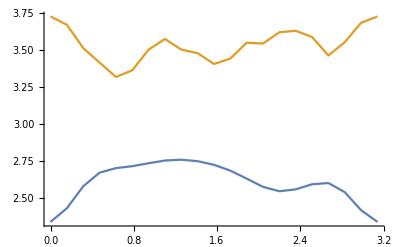

```mathematica
ListLinePlot[{rd16mean,rd16max}]
```

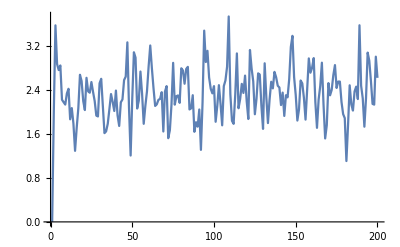

```mathematica
ListLinePlot[rd16n[[1]]]
```

## dt = pi/32

#### data

```mathematica
rd32={-0.000000000000000000*10^+00,2.000000000000000000*10^+00,3.889473931736897150*10^+00,2.535963001550383122*10^+00,1.599511874410691981*10^+00,2.462452134173275908*10^+00,3.169694596710698420*10^+00,2.578562356776703979*10^+00,1.828576623580031146*10^+00,2.044855033696050040*10^+00,2.681980450650082837*10^+00,2.506840649820263778*10^+00,1.883029619011669986*10^+00,1.744576591734770643*10^+00,2.063677199045316435*10^+00,2.421432933638047569*10^+00,2.332695682749067689*10^+00,2.137700448503696116*10^+00,2.247545498676528197*10^+00,2.271130621003958794*10^+00,2.069444526043813681*10^+00,2.129436162066402183*10^+00,2.570814901544479447*10^+00,2.630824341921726983*10^+00,2.593646683059231073*10^+00,2.447470003695104701*10^+00,2.480601654497311959*10^+00,2.241382426816747930*10^+00,1.923324107794958326*10^+00,2.055474626696240925*10^+00,3.153367074967720285*10^+00,2.676399171072992633*10^+00,1.804704454729331387*10^+00,2.418424552190034049*10^+00,2.886822140150110627*10^+00,2.592447708934226824*10^+00,2.534392512851227242*10^+00,2.656971373252694057*10^+00,2.777631714750166125*10^+00,2.731537326792655485*10^+00,1.966340151226258826*10^+00,1.574044900855663398*10^+00,2.508483860776089980*10^+00,2.764713497030903522*10^+00,2.340465409519090212*10^+00,1.961093449870227712*10^+00,2.461167306915382991*10^+00,3.084117171159512338*10^+00,1.793157051147854730*10^+00,1.939847530481235260*10^+00,2.443174015957499279*10^+00,2.670783306082229025*10^+00,2.188420563861618540*10^+00,1.456196764210279992*10^+00,2.500194411819648632*10^+00,3.321314681354453402*10^+00,2.551621490803716252*10^+00,2.027623363337392348*10^+00,3.025342356880826866*10^+00,3.490395907867125835*10^+00,2.268743394624660681*10^+00,1.605463312912409624*10^+00,2.374879014317611947*10^+00,2.784817567381006498*10^+00,2.299533943593189633*10^+00,2.201064220844101804*10^+00,2.611137628579858205*10^+00,2.354374802735953232*10^+00,1.982490847373346465*10^+00,2.131740074445831024*10^+00,2.785494785309434285*10^+00,2.405182323845179493*10^+00,1.312936906014693372*10^+00,1.965270698781649950*10^+00,3.147895709548445886*10^+00,3.104652158193721867*10^+00,2.452823930284980580*10^+00,2.434185784558681398*10^+00,2.619859400525535786*10^+00,2.091445368657655735*10^+00,1.571475136219687041*10^+00,2.494259157301236485*10^+00,2.893903053422358873*10^+00,2.213949541912760388*10^+00,2.178878351656310830*10^+00,2.591469219701676430*10^+00,2.766107628876124380*10^+00,2.925639825657808668*10^+00,2.666618491479296527*10^+00,2.397750258184744077*10^+00,2.687103868646143923*10^+00,2.910687853284366966*10^+00,2.667820685209798537*10^+00,2.600385062720890872*10^+00,2.745844249475130283*10^+00,2.380093371792550982*10^+00,1.854535515976254434*10^+00,1.983980723165007731*10^+00,2.723069959930214612*10^+00,2.860584951192987724*10^+00,2.336383283235608399*10^+00,2.664283406281927391*10^+00,3.409360664859581558*10^+00,2.641651253123263210*10^+00,1.474524836599901745*10^+00,1.682005128107164627*10^+00,2.670645399460441105*10^+00,3.145847890008333536*10^+00,2.114346603167243988*10^+00,2.410061800373286545*10^+00,2.684045253399303554*10^+00,2.312070378746323485*10^+00,2.187085546615021414*10^+00,2.058378742468278677*10^+00,2.687240120845525659*10^+00,2.351039507412404195*10^+00,1.940905895141344040*10^+00,2.010285763693589800*10^+00,2.488219025598221723*10^+00,2.876327042275702794*10^+00,2.508811628035330088*10^+00,2.577058057955133652*10^+00,3.198574770013838720*10^+00,3.085199177370402168*10^+00,2.200222001701351182*10^+00,1.980574767396624303*10^+00,2.663021853567664632*10^+00,2.214733972312384669*10^+00,1.682778600823690240*10^+00,2.413937263013476553*10^+00,3.175280460843450392*10^+00,2.432450499912344632*10^+00,1.556288277842480472*10^+00,2.306004687701976419*10^+00,2.938223226634304908*10^+00,2.779185327965811858*10^+00,1.816678584372382055*10^+00,1.446574145227955022*10^+00,2.799160898629315497*10^+00,2.891463529989216852*10^+00,2.064857952517431983*10^+00,1.930585209415470960*10^+00,2.580442012891476011*10^+00,2.348911860339070845*10^+00,1.641551106443088104*10^+00,2.202750261097721651*10^+00,3.227266737103902994*10^+00,2.748041813276070222*10^+00,2.068517882813361908*10^+00,2.296592585240199824*10^+00,2.976691559006519494*10^+00,1.865663526031406061*10^+00,1.532731647181509338*10^+00,2.852209401447773018*10^+00,3.315810702999908433*10^+00,2.453210102983169438*10^+00,1.652263946626042701*10^+00,2.222092240590316514*10^+00,2.897665408698238299*10^+00,2.653478933408844220*10^+00,1.944197633493084165*10^+00,2.671343545604687009*10^+00,3.616147801973650378*10^+00,2.133974171776817919*10^+00,7.218545326042403731*10^-01,2.021793234878745515*10^+00,3.124738061029058489*10^+00,2.274402024719021753*10^+00,1.344097861522077331*10^+00,2.054093941463513762*10^+00,3.553785101814434189*10^+00,2.184016814049961397*10^+00,1.372558583067309490*10^+00,2.192903731846915782*10^+00,3.010724408818346909*10^+00,2.202509909654421616*10^+00,1.038696338488501292*10^+00,2.322641757763424852*10^+00,3.525049086466913728*10^+00,2.228263039840918669*10^+00,1.364457533264640254*10^+00,2.114842060736776386*10^+00,2.731364646657532091*10^+00,2.644119180001075264*10^+00,2.119930691284662938*10^+00,2.321837608546501119*10^+00,2.699840473793698514*10^+00,2.540070555434585486*10^+00,2.091729392400811793*10^+00,2.008167396165096985*10^+00,2.063520406304712118*10^+00,2.414992626455956692*10^+00,2.463253738401488313*10^+00,2.421758673251037219*10^+00,2.723274645098447078*10^+00,2.351050679260002330*10^+00,1.799958573385932459*10^+00,2.231407629742311549*10^+00,2.219991028471605787*10^+00,2.169543004595626989*10^+00,2.722912528242654327*10^-14,1.997312964395158374*10^+00,3.884243528694934611*10^+00,2.765721501433906937*10^+00,1.851868128929976542*10^+00,2.598852501443087881*10^+00,3.150679344903708934*10^+00,2.638965569712443227*10^+00,1.931341664892532561*10^+00,2.061287193099349935*10^+00,2.624544473835588754*10^+00,2.572208652895590753*10^+00,2.045796929696037658*10^+00,1.882474265585896589*10^+00,2.055798859940024315*10^+00,2.471480285270008181*10^+00,2.439893852914295724*10^+00,2.306122260521282108*10^+00,2.368859597097070946*10^+00,2.416810373564335812*10^+00,2.238263399405974852*10^+00,2.223232605341340040*10^+00,2.521786444379483072*10^+00,2.634103069532117924*10^+00,2.695694256972735126*10^+00,2.584188125823509985*10^+00,2.579327876312505818*10^+00,2.387968194572843483*10^+00,2.111468345626399845*10^+00,2.200521706043271575*10^+00,3.139091555904259145*10^+00,2.663475019437460123*10^+00,1.827482962885113915*10^+00,2.430808652713865481*10^+00,2.876628914391419656*10^+00,2.642903963351209917*10^+00,2.665786188350170782*10^+00,2.797709274176417349*10^+00,2.905488135906944880*10^+00,2.813489468243195013*10^+00,2.071478745187251391*10^+00,1.661041903074552906*10^+00,2.462936566067600808*10^+00,2.791144162552638086*10^+00,2.451088590594225458*10^+00,2.100030138947726055*10^+00,2.509354062052880252*10^+00,3.056145369372881504*10^+00,1.924254013661777174*10^+00,2.060557249799261914*10^+00,2.478706251618434830*10^+00,2.707056131139868871*10^+00,2.310534638252546902*10^+00,1.679176799485547544*10^+00,2.594140208654245772*10^+00,3.340425509715290175*10^+00,2.718825785899566583*10^+00,2.257176966915222849*10^+00,3.118517402010240858*10^+00,3.451589844564074472*10^+00,2.429354141392965794*10^+00,1.852997208640846827*10^+00,2.522523310740784286*10^+00,2.768365559805431531*10^+00,2.293885286960672065*10^+00,2.250087855525620295*10^+00,2.677321186788684138*10^+00,2.472685123728750156*10^+00,2.143689555087909593*10^+00,2.353464846106370523*10^+00,2.946655250332575804*10^+00,2.484189232003810588*10^+00,1.384131982590472321*10^+00,2.052792176990952733*10^+00,3.165939669755291508*10^+00,3.150618966528171416*10^+00,2.636723219287437470*10^+00,2.586286099282840034*10^+00,2.647464555268015829*10^+00,2.122593706420327742*10^+00,1.636143326205864890*10^+00,2.526872113443459966*10^+00,2.916575742134224658*10^+00,2.296825123191488682*10^+00,2.317946929057696615*10^+00,2.764594807640040841*10^+00,2.835641776334657305*10^+00,2.893147875665533331*10^+00,2.703543338027551535*10^+00,2.504093346047896240*10^+00,2.767227836081037395*10^+00,2.988394988269593711*10^+00,2.803834942486565840*10^+00,2.688377405709180490*10^+00,2.829177865664168845*10^+00,2.549171115653535935*10^+00,2.047538166633190215*10^+00,2.169570774396061719*10^+00,2.774351345266312663*10^+00,2.769354952785941126*10^+00,2.341042671186226887*10^+00,2.693779565021664268*10^+00,3.381291363972612096*10^+00,2.765198586434378214*10^+00,1.707672666610524193*10^+00,1.863968364720020920*10^+00,2.814885803085276805*10^+00,3.138472693390403911*10^+00,2.222833197243870629*10^+00,2.531751415224428925*10^+00,2.737050349853794806*10^+00,2.364328357278681736*10^+00,2.268933556627915848*10^+00,2.160579187113794486*10^+00,2.708128807772585134*10^+00,2.335847794867862870*10^+00,1.980156317128112464*10^+00,2.055531660645780079*10^+00,2.410068853862564531*10^+00,2.830299913617194463*10^+00,2.609897117883863693*10^+00,2.750218327266268581*10^+00,3.247314097060222338*10^+00,3.138956025500487357*10^+00,2.430938949242578140*10^+00,2.207269720599937202*10^+00,2.707589676969144321*10^+00,2.199492157868903508*10^+00,1.713745005919503850*10^+00,2.441282880511206343*10^+00,3.150570507939831622*10^+00,2.510819380618329433*10^+00,1.785736677976065501*10^+00,2.494015943651996636*10^+00,2.983517375250488879*10^+00,2.771473449337837902*10^+00,1.940429942517437389*10^+00,1.597061348883835885*10^+00,2.855685627655132564*10^+00,2.997016002317514527*10^+00,2.238346827557300855*10^+00,2.084795665799052067*10^+00,2.625786610946427402*10^+00,2.368057251877722091*10^+00,1.695400635988920879*10^+00,2.257597841912478476*10^+00,3.232574941015686321*10^+00,2.785019828853001478*10^+00,2.190844997730694743*10^+00,2.399174388753397391*10^+00,2.952493728167468579*10^+00,2.045290214784575511*10^+00,1.731967009558743609*10^+00,2.932363039379099146*10^+00,3.357684347662557744*10^+00,2.617057715861529577*10^+00,1.930206502464865137*10^+00,2.382257145535481957*10^+00,2.889962259784093046*10^+00,2.634206689327298623*10^+00,1.972663721932173875*10^+00,2.673950757498428032*10^+00,3.580821041070382904*10^+00,2.298769136332599050*10^+00,9.959125182101633555*10^-01,2.216430533549529791*10^+00,3.152041490200415019*10^+00,2.397049112866486364*10^+00,1.541439254877721599*10^+00,2.152724376247511007*10^+00,3.460322985596143930*10^+00,2.250914876920568908*10^+00,1.506252641674724391*10^+00,2.269216080729753671*10^+00,3.012249586865082485*10^+00,2.317594272348837414*10^+00,1.212778418966749427*10^+00,2.440203136508686033*10^+00,3.495028388533672814*10^+00,2.304704164678892830*10^+00,1.534937636754658108*10^+00,2.180616693730394573*10^+00,2.678879661996875772*10^+00,2.650339297179201470*10^+00,2.202900869224224678*10^+00,2.461610718861745095*10^+00,2.806510368195760385*10^+00,2.670491522476202917*10^+00,2.264305758825236214*10^+00,2.142902827996485016*10^+00,2.079427864320555486*10^+00,2.362426352739766866*10^+00,2.382577473813427105*10^+00,2.492183161820666015*10^+00,2.828808173591477182*10^+00,2.537111953746003401*10^+00,2.023024310371277057*10^+00,2.371350181024583836*10^+00,2.269090066053901733*10^+00,2.178432220561062671*10^+00,-9.610279511444755881*10^-16,1.989519616320031270*10^+00,3.869137723225628989*10^+00,3.042257979889137154*10^+00,2.204390357498696051*10^+00,2.749677663092416680*10^+00,3.091663005928836583*10^+00,2.732558224605171393*10^+00,2.159971952799274231*10^+00,2.101461724521795915*10^+00,2.469478036041622637*10^+00,2.677639887657946804*10^+00,2.281982622507028768*10^+00,2.098672699302386313*10^+00,2.069077977595514373*10^+00,2.584098728419343072*10^+00,2.677894249739462218*10^+00,2.554453626307805258*10^+00,2.573512138835560403*10^+00,2.654267646579187456*10^+00,2.499737312861436411*10^+00,2.335021327886308118*10^+00,2.409280669983068002*10^+00,2.629431270291971323*10^+00,2.916899601746928195*10^+00,2.781467938144311702*10^+00,2.655560046167960042*10^+00,2.630698895623788225*10^+00,2.447099525311719148*10^+00,2.409416233364264581*10^+00,3.065922342705231785*10^+00,2.581493222378066665*10^+00,1.903890043206652116*10^+00,2.478158385533809849*10^+00,2.840325997429502536*10^+00,2.680411997720237860*10^+00,2.856150866163413404*10^+00,2.969341836714422200*10^+00,3.017406152850234946*10^+00,2.974663624101623327*10^+00,2.334412538621463806*10^+00,1.863260726489766483*10^+00,2.345267071684686844*10^+00,2.804676952908458532*10^+00,2.679263569917350374*10^+00,2.356290783368030883*10^+00,2.586908065774539800*10^+00,2.982755778186552575*10^+00,2.156819970493436767*10^+00,2.275465869715396661*10^+00,2.534477147934522279*10^+00,2.734113215189716950*10^+00,2.557512259964177304*10^+00,2.092364230488899857*10^+00,2.723589694580893728*10^+00,3.358759589816088909*10^+00,3.022712499585089585*10^+00,2.678509004995494713*10^+00,3.320801775875775963*10^+00,3.396938554875666760*10^+00,2.667411013661793007*10^+00,2.253653671149646431*10^+00,2.752086761864661835*10^+00,2.742065409918433616*10^+00,2.297708031380509386*10^+00,2.380241392353204866*10^+00,2.817643229844117414*10^+00,2.630504644135530867*10^+00,2.415342008884773239*10^+00,2.695391546517498682*10^+00,3.196464682794867063*10^+00,2.563704364745748698*10^+00,1.486038521865699291*10^+00,2.203565647586487319*10^+00,3.174235835348811818*10^+00,3.232533192925626686*10^+00,2.909211499900866471*10^+00,2.811960376375285175*10^+00,2.619153642270192428*10^+00,2.149538296618091149*10^+00,1.763999488977155528*10^+00,2.611532806405756801*10^+00,2.967171648925813976*10^+00,2.410420789490726357*10^+00,2.496211654245183986*10^+00,3.033921186770914602*10^+00,2.928524370489084205*10^+00,2.797103020937933060*10^+00,2.734569062162166997*10^+00,2.679200453490364175*10^+00,2.893401452420101716*10^+00,3.173248151941839179*10^+00,3.035631365712160523*10^+00,2.849293889862881457*10^+00,2.957611784716932313*10^+00,2.754742227338377702*10^+00,2.378238886898750071*10^+00,2.521515297041802217*10^+00,2.858466977786110252*10^+00,2.576881705467725769*10^+00,2.273310078833992609*10^+00,2.725265292486651170*10^+00,3.311493754616477769*10^+00,2.913601312001692811*10^+00,2.194522149207439821*10^+00,2.197251519082620952*10^+00,3.007188088828567363*10^+00,3.106936928762465744*10^+00,2.336170614541944079*10^+00,2.734328326924750918*10^+00,2.840652351937621667*10^+00,2.465172554873908961*10^+00,2.434493518064069661*10^+00,2.367299676428028299*10^+00,2.734724203502335360*10^+00,2.319623978028466205*10^+00,2.059104766002836318*10^+00,2.145131150155662247*10^+00,2.266272750896622057*10^+00,2.772407986126647739*10^+00,2.816472318215089476*10^+00,3.004829654626739011*10^+00,3.303379808543918994*10^+00,3.248559755805652038*10^+00,2.825379934999027842*10^+00,2.549247366499384881*10^+00,2.761534427805656833*10^+00,2.170617443103092459*10^+00,1.830863065788882249*10^+00,2.515567313606386080*10^+00,3.108946463585486431*10^+00,2.622814900780331193*10^+00,2.135358749318977178*10^+00,2.756629411039354327*10^+00,3.018280819741228083*10^+00,2.760267513043888066*10^+00,2.238113207222701462*10^+00,1.928404965668374604*10^+00,2.922908309739427501*10^+00,3.182202509900593945*10^+00,2.512569351261649153*10^+00,2.280437590038050466*10^+00,2.663568469235240155*10^+00,2.408719724493167291*10^+00,1.844976346073478268*10^+00,2.377385184851359412*10^+00,3.225183127197009725*10^+00,2.835206851607489753*10^+00,2.359350808865016358*10^+00,2.539957863550355466*10^+00,2.891699555854992276*10^+00,2.331225835747942732*10^+00,2.057785019177415631*10^+00,3.056645220166482435*10^+00,3.442727039935880029*10^+00,2.871885132459113699*10^+00,2.397747565749159371*10^+00,2.631546729985683175*10^+00,2.817757487934507310*10^+00,2.518018916853183242*10^+00,2.058587542162450212*10^+00,2.714959682200976054*10^+00,3.509603585498799028*10^+00,2.569177753135637232*10^+00,1.518217567093493425*10^+00,2.549043858758477832*10^+00,3.183847440991328437*10^+00,2.569644677972137359*10^+00,1.953652813928918430*10^+00,2.326576531891162425*10^+00,3.245350578668120711*10^+00,2.412309127298375877*10^+00,1.780915934897465469*10^+00,2.406312067605455240*10^+00,3.019547517141922821*10^+00,2.457556266761146802*10^+00,1.546377006694809042*10^+00,2.668279028545386566*10^+00,3.411489153315024669*10^+00,2.449627032579869912*10^+00,1.913679001433547633*10^+00,2.339260302914089706*10^+00,2.586545910730416509*10^+00,2.647062669908054389*10^+00,2.412316497651090685*10^+00,2.744340486857603345*10^+00,2.980888658650406864*10^+00,2.891067760000805009*10^+00,2.509925142205267967*10^+00,2.381588870625039434*10^+00,2.141061532166928849*10^+00,2.255535242504625337*10^+00,2.228298233181234433*10^+00,2.597937136089762067*10^+00,3.092550038351641106*10^+00,2.811154264197485819*10^+00,2.360865862031412021*10^+00,2.553511599874425997*10^+00,2.400016000052399345*10^+00,2.183572235637392112*10^+00,9.610279511444749964*10^-16,1.977395258237991449*10^+00,3.845785922085721786*10^+00,3.185852375713541740*10^+00,2.453273557510147196*10^+00,2.784674061709004889*10^+00,2.999960024062052533*10^+00,2.761312017096170024*10^+00,2.375478440908264766*10^+00,2.155778189497655539*10^+00,2.359199405598700672*10^+00,2.722662836930013874*10^+00,2.442797216156623819*10^+00,2.281839784888755496*10^+00,2.189781754514801282*10^+00,2.741034138144932797*10^+00,2.867484712226272769*10^+00,2.717205639604408862*10^+00,2.764630146969373481*10^+00,2.864000047348858935*10^+00,2.674765937275131122*10^+00,2.314653359126467080*10^+00,2.284767933384311611*10^+00,2.686583427615619968*10^+00,3.068942490400359713*10^+00,2.831438508093055528*10^+00,2.641082401992724371*10^+00,2.821041642596818555*10^+00,2.697653251443225209*10^+00,2.484257571567269007*10^+00,2.903468861592845229*10^+00,2.421240927731393100*10^+00,1.978708150954923584*10^+00,2.519196079038505509*10^+00,2.761121159458884478*10^+00,2.644677930743195127*10^+00,2.936653324399681075*10^+00,3.037602749310389871*10^+00,2.980529510648612934*10^+00,3.083554144414748510*10^+00,2.645987745443471262*10^+00,2.027709721651334451*10^+00,2.202136673834727887*10^+00,2.794121745700307358*10^+00,2.830221671354173907*10^+00,2.485967869893497717*10^+00,2.560505792925608315*10^+00,2.862110429964294767*10^+00,2.343387807302486081*10^+00,2.453670425732125793*10^+00,2.548763449475335285*10^+00,2.683002689087234494*10^+00,2.818966936057826445*10^+00,2.474924715209302573*10^+00,2.809138435728241845*10^+00,3.338467477210558254*10^+00,3.276869433474669524*10^+00,3.028981865002116969*10^+00,3.437899730393625397*10^+00,3.364860063658151823*10^+00,2.766466153888563095*10^+00,2.488664804555225540*10^+00,2.856141655033707316*10^+00,2.760685941925191678*10^+00,2.373954644398433622*10^+00,2.508712180737682207*10^+00,2.963674693586498154*10^+00,2.741400458272819751*10^+00,2.579495962112292151*10^+00,2.918844270295864796*10^+00,3.312093403726815044*10^+00,2.573632839493994240*10^+00,1.588683398122536783*10^+00,2.296222382289673014*10^+00,3.164325388099176628*10^+00,3.281004982483025412*10^+00,3.078644386797848131*10^+00,2.915514381920859766*10^+00,2.459799923182339754*10^+00,2.065579916432712437*10^+00,1.844736786094985481*10^+00,2.672785239572457616*10^+00,3.058588564215852124*10^+00,2.481040914067631498*10^+00,2.608354174340502318*10^+00,3.196755492805383625*10^+00,2.906041598521696301*10^+00,2.620217337164473470*10^+00,2.718915959123831438*10^+00,2.761499494128718535*10^+00,2.927139336234284794*10^+00,3.297580844838691849*10^+00,3.190866146176603024*10^+00,2.950089178454339489*10^+00,3.031101540842990438*10^+00,2.858060312232708178*10^+00,2.661717986306657124*10^+00,2.792537162531975703*10^+00,2.858851940013895643*10^+00,2.403514792257762878*10^+00,2.186685032348431257*10^+00,2.706620427883445146*10^+00,3.189592403552875322*10^+00,3.015043309274078265*10^+00,2.664685981248288371*10^+00,2.473567281612083946*10^+00,3.078758926437092924*10^+00,3.005044960731340975*10^+00,2.339202572686405635*10^+00,2.837497969301056244*10^+00,2.955566960900183560*10^+00,2.571840045550175979*10^+00,2.570767716816809934*10^+00,2.559913292899236303*10^+00,2.777006969457445962*10^+00,2.360198271388680435*10^+00,2.149493739234511036*10^+00,2.211350135064841016*10^+00,2.128887510535507843*10^+00,2.736615313977760700*10^+00,2.963700576861380220*10^+00,3.110623269153924397*10^+00,3.288394312503518879*10^+00,3.304581460565828799*10^+00,3.103869675724194366*10^+00,2.745672890126262367*10^+00,2.730880437340455824*10^+00,2.198329309647119700*10^+00,1.965181590479633034*10^+00,2.615942164253701741*10^+00,3.071260813458885686*10^+00,2.677235361753011134*10^+00,2.381169352524437066*10^+00,2.837019611842622080*10^+00,2.887041342520127341*10^+00,2.698231253848009548*10^+00,2.551739681557787520*10^+00,2.226622038083347910*10^+00,2.920605418068336512*10^+00,3.327078335595303749*10^+00,2.688877431051826861*10^+00,2.313400095373423504*10^+00,2.538021801764983820*10^+00,2.436209055018947023*10^+00,2.037243666088459637*10^+00,2.521097684739351585*10^+00,3.178892221855826428*10^+00,2.817998240813354371*10^+00,2.407459016796259288*10^+00,2.584996123545707292*10^+00,2.826851386496139540*10^+00,2.557749234334583122*10^+00,2.357206455897781439*10^+00,3.121458653407105821*10^+00,3.443554628468610712*10^+00,3.062331767251630588*10^+00,2.780882388180278220*10^+00,2.786357716656037820*10^+00,2.626763711780990995*10^+00,2.270595071153096001*10^+00,2.089677428115098046*10^+00,2.756031508899669635*10^+00,3.448964420131260145*10^+00,2.778217201144479009*10^+00,1.977792775248416124*10^+00,2.842671720103824740*10^+00,3.125980936474573646*10^+00,2.601525955082529151*10^+00,2.227791515857417970*10^+00,2.480750446326953629*10^+00,3.044217840423851129*10^+00,2.594989817236863949*10^+00,2.089992704246351529*10^+00,2.475907940478018432*10^+00,2.993822463142436163*10^+00,2.527796141524256690*10^+00,1.851090976985082071*10^+00,2.846278148992388513*10^+00,3.287956619188973750*10^+00,2.577945559637778938*10^+00,2.296687371875294481*10^+00,2.542026196777950275*10^+00,2.536411111602564272*10^+00,2.633557772430737742*10^+00,2.614219471840185438*10^+00,3.013742657861788299*10^+00,3.187350647602170461*10^+00,3.032427648431716971*10^+00,2.646934135970126167*10^+00,2.616018136647561221*10^+00,2.326556299690336616*10^+00,2.216834520138895037*10^+00,2.095971766855142970*10^+00,2.691319875566573483*10^+00,3.315687546901019633*10^+00,2.964593356341969077*10^+00,2.569219636016101482*10^+00,2.630978362415111071*10^+00,2.535111916360729190*10^+00,2.188906814291761371*10^+00,4.805139755722374982*10^-16,1.962142191318804407*10^+00,3.816558188097141979*10^+00,3.153093983344072981*10^+00,2.568015746366675955*10^+00,2.794718108634268283*10^+00,2.920333480751796884*10^+00,2.715689742205195323*10^+00,2.462409676557669513*10^+00,2.230652211946513752*10^+00,2.353991930422558276*10^+00,2.733285667267929764*10^+00,2.531615195890465131*10^+00,2.477516917435920618*10^+00,2.422367299439032173*10^+00,2.884318975657830464*10^+00,2.953561556309202807*10^+00,2.804343330104304588*10^+00,2.934047061347051066*10^+00,2.966492428814508919*10^+00,2.700638366787905031*10^+00,2.231984207934979203*10^+00,2.306352393799663059*10^+00,2.798898203860107348*10^+00,3.091589967915160386*10^+00,2.759238849288946582*10^+00,2.679940927522753036*10^+00,2.937855634706565411*10^+00,2.819391477308345273*10^+00,2.464093568291916725*10^+00,2.688069757356132516*10^+00,2.335440199710909770*10^+00,2.097388660814781147*10^+00,2.587096165719394047*10^+00,2.640979515789051657*10^+00,2.614049315911491256*10^+00,2.864159120963640337*10^+00,2.941853188858120305*10^+00,2.817708560718458877*10^+00,3.138099767511894456*10^+00,2.929670658521359883*10^+00,2.124805911252717561*10^+00,2.144913330076756885*10^+00,2.804521650417007628*10^+00,2.828870103633917665*10^+00,2.429117703779256399*10^+00,2.436287889702186238*10^+00,2.732250557732425200*10^+00,2.459236494251212601*10^+00,2.562922515884145547*10^+00,2.532817651293992611*10^+00,2.585327946076605876*10^+00,2.958363412168676376*10^+00,2.727907117309188223*10^+00,2.855917734520676987*10^+00,3.313077534218065612*10^+00,3.405647855013131498*10^+00,3.206679413488476627*10^+00,3.437437532332072276*10^+00,3.298135407486440407*10^+00,2.686024081220360848*10^+00,2.452720806584169466*10^+00,2.799591400702733157*10^+00,2.877880916787234789*10^+00,2.613252984474668139*10^+00,2.594724872297064167*10^+00,3.045769268177146660*10^+00,2.814322849888510447*10^+00,2.669270174128004491*10^+00,2.985096690997191438*10^+00,3.270029020053574875*10^+00,2.534718697617340588*10^+00,1.641218690883179177*10^+00,2.366965735680085725*10^+00,3.187528217464151936*10^+00,3.297580949916575577*10^+00,3.139010587806898123*10^+00,2.930920449640856074*10^+00,2.294271510276400861*10^+00,1.895994038594376541*10^+00,1.801527184191461073*10^+00,2.703715452932196950*10^+00,3.236039141380139483*10^+00,2.556087218688539942*10^+00,2.663793709483721628*10^+00,3.247945212720086516*10^+00,2.811634734774632882*10^+00,2.439048126860988042*10^+00,2.657048530662556196*10^+00,2.746150038129692383*10^+00,2.885750584178134570*10^+00,3.307982629871421665*10^+00,3.222492691207788695*10^+00,3.016461967592380056*10^+00,3.038883513481462018*10^+00,2.866856469411486419*10^+00,2.831735118967975584*10^+00,2.921991066536797188*10^+00,2.832317889375162601*10^+00,2.404591563973746737*10^+00,2.259572286773182004*10^+00,2.675290846257587507*10^+00,3.041114772007943667*10^+00,3.049344766094389758*10^+00,2.981990311836787200*10^+00,2.610723811364782598*10^+00,3.064899016702263168*10^+00,2.902867464848936763*10^+00,2.263863103637886010*10^+00,2.844400471519410445*10^+00,3.088886199495894047*10^+00,2.709469886893451029*10^+00,2.684073891626980402*10^+00,2.736739616298132560*10^+00,2.811504780771056922*10^+00,2.461893520343525932*10^+00,2.302591584792169854*10^+00,2.263182771705644747*10^+00,2.112577741193267133*10^+00,2.780529312757848981*10^+00,3.064432395091897909*10^+00,3.121516117827737080*10^+00,3.213715565766253057*10^+00,3.306008925510512064*10^+00,3.181925059493769581*10^+00,2.759451112661276184*10^+00,2.688348870750115527*10^+00,2.332053053051910574*10^+00,2.138161630938701041*10^+00,2.695047643098726908*10^+00,3.004379858870724451*10^+00,2.728408307836645008*10^+00,2.494842969389386766*10^+00,2.749688974564094224*10^+00,2.665934370831380296*10^+00,2.666256798972710840*10^+00,2.803409391900086867*10^+00,2.387464604081812158*10^+00,2.868828111576072981*10^+00,3.394100407999601998*10^+00,2.707885949596458897*10^+00,2.126897992614425359*10^+00,2.249858696509927203*10^+00,2.383841319843401418*10^+00,2.209794401145949827*10^+00,2.646300466528237472*10^+00,3.105391280214235827*10^+00,2.765200248448565823*10^+00,2.404414861957606231*10^+00,2.532423438523425219*10^+00,2.721895143188292288*10^+00,2.656612377846650830*10^+00,2.572310668121512656*10^+00,3.134182240876484116*10^+00,3.402132487837215447*10^+00,3.138678420727111451*10^+00,2.985949667714806743*10^+00,2.865707360902961742*10^+00,2.459310391299911025*10^+00,2.058148361995224551*10^+00,2.056536255897957854*10^+00,2.797726877232837417*10^+00,3.426679131901471109*10^+00,2.875475328107380157*10^+00,2.301662114026626238*10^+00,3.071408803675802268*10^+00,2.984382148570913884*10^+00,2.487028404429084905*10^+00,2.291085858568953526*10^+00,2.591678679977087008*10^+00,2.995706157861242058*10^+00,2.758653187598947287*10^+00,2.400697935798301597*10^+00,2.514335766559763208*10^+00,2.934463709904756357*10^+00,2.555130131836328644*10^+00,2.126164709706222844*10^+00,2.885865641319624419*10^+00,3.136943262728277837*10^+00,2.663884845293309045*10^+00,2.565701348219199041*10^+00,2.727032984261320792*10^+00,2.556069625422598968*10^+00,2.641545717562436835*10^+00,2.740523356931532817*10^+00,3.194644873553830866*10^+00,3.358716247212107930*10^+00,3.092543384419859986*10^+00,2.668042691248146525*10^+00,2.860403174604527976*10^+00,2.687733893934857843*10^+00,2.306491309633333042*10^+00,2.076812723906789948*10^+00,2.773500706250890069*10^+00,3.380435358082510167*10^+00,2.967623503062019719*10^+00,2.607132349201538801*10^+00,2.617679062897381392*10^+00,2.626856770475559433*10^+00,2.170522122669244158*10^+00,3.203426503814917641*10^-16,1.945266182126420107*10^+00,3.784247627111740453*10^+00,3.014467178618978060*10^+00,2.608586439962327752*10^+00,2.993502232263416829*10^+00,2.903286044817788625*10^+00,2.632475866422104183*10^+00,2.384951009366213626*10^+00,2.291694754830759351*10^+00,2.448547074718359529*10^+00,2.777712246887581671*10^+00,2.618202440989545021*10^+00,2.697743563733232985*10^+00,2.704162684097568992*10^+00,3.027651911135953000*10^+00,2.960975757824072740*10^+00,2.885883754740919294*10^+00,3.030796622061165735*10^+00,2.961869564936108645*10^+00,2.642172364050455080*10^+00,2.199381310854803484*10^+00,2.442090915287723707*10^+00,2.934752079997762664*10^+00,3.025251043347223057*10^+00,2.686106382180481145*10^+00,2.741838250373560548*10^+00,2.997523199415592643*10^+00,2.865980827216272786*10^+00,2.480140726713885080*10^+00,2.541472793121335449*10^+00,2.357076282658388422*10^+00,2.280703032654979978*10^+00,2.667695672824821340*10^+00,2.620356443606220331*10^+00,2.638594891311376589*10^+00,2.697526406366440810*10^+00,2.785176098762497610*10^+00,2.621748926248983480*10^+00,3.194635144792033365*10^+00,3.145107515891682581*10^+00,2.171456074586487706*10^+00,2.218697626967526926*10^+00,2.871891858481522952*10^+00,2.724660801701526580*10^+00,2.248476232472786052*10^+00,2.248436701505856838*10^+00,2.602910766118524677*10^+00,2.525870848079971864*10^+00,2.585967104110330261*10^+00,2.485863640797592478*10^+00,2.518682634155855915*10^+00,2.962465320418214976*10^+00,2.849867240512686806*10^+00,2.918260600719795761*10^+00,3.313498711594740964*10^+00,3.450551687605842854*10^+00,3.258316138438228204*10^+00,3.369983522315269209*10^+00,3.180913638911876617*10^+00,2.519977969454317179*10^+00,2.282697594068736624*10^+00,2.723250788037790748*10^+00,3.033943514824623655*10^+00,2.920602474063282994*10^+00,2.651076278604769243*10^+00,3.022353031496459508*10^+00,2.853507459815425751*10^+00,2.758020151178692370*10^+00,3.005857710164177021*10^+00,3.151880270564012765*10^+00,2.445248019199735889*10^+00,1.690893794130120309*10^+00,2.441478247361048126*10^+00,3.281096043640856053*10^+00,3.292755929737788190*10^+00,3.139391234469886438*10^+00,2.929865043215228226*10^+00,2.274845909074311390*10^+00,1.741205088488307906*10^+00,1.669816328940163519*10^+00,2.652728899584640754*10^+00,3.399454635685826176*10^+00,2.689232772922230730*10^+00,2.719955010388910743*10^+00,3.251724424792109325*10^+00,2.737634513075210663*10^+00,2.445156947807616721*10^+00,2.585868223180134429*10^+00,2.674833221023996011*10^+00,2.851129541432526171*10^+00,3.212578001772517844*10^+00,3.167399241060835813*10^+00,3.072637569601183838*10^+00,3.029485336303620269*10^+00,2.861023661122914952*10^+00,2.934527039364250633*10^+00,2.926510374159066785*10^+00,2.785849042775688567*10^+00,2.575203442227785189*10^+00,2.475544849757342902*10^+00,2.650929278891985152*10^+00,2.898088500691729408*10^+00,3.025663065341810842*10^+00,3.125677145589046191*10^+00,2.686620463440908324*10^+00,3.037798399438764285*10^+00,2.852469651658570804*10^+00,2.223475529095372938*10^+00,2.789292414097203743*10^+00,3.212370303632432922*10^+00,2.827514126444998332*10^+00,2.816322054987245860*10^+00,2.905884677060464938*10^+00,2.886060887698855826*10^+00,2.651317473466200170*10^+00,2.498895624105887059*10^+00,2.338816613869344252*10^+00,2.244753742286534681*10^+00,2.898609674411520842*10^+00,3.127261855615126596*10^+00,3.086242481399434023*10^+00,3.158905804776918291*10^+00,3.298277047162597064*10^+00,3.110785732212213439*10^+00,2.673137156152662008*10^+00,2.767810408636941055*10^+00,2.518303275976998989*10^+00,2.335135044362335321*10^+00,2.747197716034997406*10^+00,2.979551863540150780*10^+00,2.780292696467598468*10^+00,2.521145161914617461*10^+00,2.577098563796967667*10^+00,2.519243610018678137*10^+00,2.715012449726217802*10^+00,3.031791135972042195*10^+00,2.435263750218069845*10^+00,2.805002208249689488*10^+00,3.437999099945804993*10^+00,2.663264830153731832*10^+00,1.870240559605800268*10^+00,1.967720346518471608*10^+00,2.288899481117416368*10^+00,2.335989304042906500*10^+00,2.734358850560295817*10^+00,3.059364752634031515*10^+00,2.734867458583374322*10^+00,2.396856272733601134*10^+00,2.498608460933672060*10^+00,2.601215240144393093*10^+00,2.642521795896215053*10^+00,2.672932401789964274*10^+00,3.149678311008132336*10^+00,3.383223874897815620*10^+00,3.124076432053675578*10^+00,3.054757346642315241*10^+00,2.922781621942057040*10^+00,2.530663072897223032*10^+00,2.072524775261977759*10^+00,2.029567785505383526*10^+00,2.783168353968870079*10^+00,3.417106179180774195*10^+00,2.874923161180322317*10^+00,2.477188920017012741*10^+00,3.212231065510573025*10^+00,2.926682059259520408*10^+00,2.342598628982338393*10^+00,2.247263945576781996*10^+00,2.717068299760929673*10^+00,3.107204116919055625*10^+00,2.929810329772194688*10^+00,2.621554093348316350*10^+00,2.504673377476570373*10^+00,2.871329477603569380*10^+00,2.587081022512953687*10^+00,2.320712007083115758*10^+00,2.811645164827147880*10^+00,3.001032167519682936*10^+00,2.721042236198353947*10^+00,2.714021984458700576*10^+00,2.866040900945833858*10^+00,2.673858081378337914*10^+00,2.676776066790211406*10^+00,2.785259553759938722*10^+00,3.272804017071325511*10^+00,3.463361237318899555*10^+00,3.120859786700655558*10^+00,2.712495762597632698*10^+00,3.088450963060058285*10^+00,3.078740679092877741*10^+00,2.475407051895095023*10^+00,2.201123798645160168*10^+00,2.879933104837542501*10^+00,3.316028915543125954*10^+00,2.838727872042700273*10^+00,2.519864000304581797*10^+00,2.619562463173060962*10^+00,2.695087813101397778*10^+00,2.148939917090928908*10^+00,-9.610279511444755881*10^-16,1.928424207011520064*10^+00,3.751846599235996838*10^+00,2.872033961081656539*10^+00,2.627025893922867894*10^+00,3.279005293193439474*10^+00,2.945207935042712499*10^+00,2.532933879278485456*10^+00,2.244379736857781360*10^+00,2.290418592664273945*10^+00,2.627539526759750110*10^+00,2.852196589544496064*10^+00,2.737203795921732130*10^+00,2.928790367379130899*10^+00,2.947330908293198437*10^+00,3.089312395706795389*10^+00,2.973884800688547436*10^+00,2.980820293282205657*10^+00,3.065444748871528624*10^+00,2.885047551132812416*10^+00,2.590071265670487399*10^+00,2.256533567064285872*10^+00,2.573148484512934875*10^+00,3.061875012461139800*10^+00,2.969909009786413367*10^+00,2.660715472337955134*10^+00,2.737279926780061157*10^+00,3.030199714170199066*10^+00,2.857666731552535033*10^+00,2.556499876493071088*10^+00,2.511814106400059643*10^+00,2.471167932367363207*10^+00,2.497116083550702026*10^+00,2.758357143163474579*10^+00,2.656383262667736389*10^+00,2.651644028742421444*10^+00,2.530585177353289694*10^+00,2.616341315637929821*10^+00,2.491096992422745515*10^+00,3.224538479611968711*10^+00,3.271942360792116311*10^+00,2.189555293896358279*10^+00,2.381979907080196135*10^+00,2.977797156181364535*10^+00,2.665558708474675242*10^+00,2.072156775080529645*10^+00,2.059321967224783112*10^+00,2.516458557889829972*10^+00,2.586138328451776047*10^+00,2.561731089288802110*10^+00,2.424274961748358770*10^+00,2.490243890161730977*10^+00,2.873585708604371902*10^+00,2.866941372874559857*10^+00,2.995692474996122900*10^+00,3.354683526193146026*10^+00,3.487967484962361642*10^+00,3.238421873428533715*10^+00,3.282914116047443098*10^+00,3.071055315726727741*10^+00,2.401434414334246092*10^+00,2.178695144639722692*10^+00,2.665567280157963292*10^+00,3.150647260753504764*10^+00,3.193017630653088634*10^+00,2.663477027441358835*10^+00,2.925231891653866878*10^+00,2.865124142668070917*10^+00,2.839180722568380499*10^+00,3.086367392171032176*10^+00,3.030385190604039991*10^+00,2.338960767076337266*10^+00,1.756847740975349570*10^+00,2.486458072501657846*10^+00,3.381064008209188732*10^+00,3.265176441231919302*10^+00,3.096002527230302892*10^+00,2.948885192321450965*10^+00,2.404827942701254884*10^+00,1.665062525897075041*10^+00,1.532312554243867586*10^+00,2.539013384278155705*10^+00,3.458518118496610061*10^+00,2.793724801360045085*10^+00,2.751498338443248759*10^+00,3.230289900259872393*10^+00,2.699561960743433353*10^+00,2.484427832365921684*10^+00,2.545822727263185481*10^+00,2.604456008621658381*10^+00,2.869683112274026726*10^+00,3.062798948159829671*10^+00,3.085096121643721823*10^+00,3.130920910051886441*10^+00,3.025710041329741085*10^+00,2.860196582064003845*10^+00,2.975034299660601622*10^+00,2.874109659177290332*10^+00,2.728833419860112741*10^+00,2.786972717812341127*10^+00,2.720393169117812260*10^+00,2.664228477741431789*10^+00,2.786650595205397263*10^+00,2.972574029675537410*10^+00,3.168576316431145568*10^+00,2.712504404363416999*10^+00,3.029801536690888142*10^+00,2.928730243101830943*10^+00,2.290960811519664020*10^+00,2.777203651945774787*10^+00,3.265045831425180012*10^+00,2.882022630156373388*10^+00,2.937300367698274961*10^+00,3.065806948676438104*10^+00,2.996506157011987526*10^+00,2.865198421777663373*10^+00,2.707330533480376111*10^+00,2.442751819379529010*10^+00,2.404244883942811217*10^+00,2.998783159431192225*10^+00,3.147826228146574756*10^+00,3.022092552220508210*10^+00,3.107457791726757179*10^+00,3.287710377920004312*10^+00,2.973620287593866873*10^+00,2.630740178954598996*10^+00,2.874187735437740532*10^+00,2.662451703547783488*10^+00,2.533288588880620473*10^+00,2.791371922821993756*10^+00,3.034411227258856592*10^+00,2.845471016090563410*10^+00,2.489764116768827140*10^+00,2.447860295535060793*10^+00,2.509569878413039135*10^+00,2.825593460937268819*10^+00,3.208743324944715702*10^+00,2.423106097059948283*10^+00,2.771978595538286072*10^+00,3.470842599267652595*10^+00,2.616520655864780220*10^+00,1.702800821600960912*10^+00,1.792331296224853210*10^+00,2.183971278071272337*10^+00,2.397038603517465116*10^+00,2.804714862131030273*10^+00,3.047491557235249449*10^+00,2.730339020768405511*10^+00,2.429140808516550898*10^+00,2.495053271518002269*10^+00,2.552942109167628981*10^+00,2.559068116281280947*10^+00,2.646964710084408257*10^+00,3.152225837567394606*10^+00,3.399275747863572672*10^+00,3.079002909462771331*10^+00,3.039159228503280019*10^+00,2.985405912293966235*10^+00,2.794607271746855748*10^+00,2.298082729785140721*10^+00,2.107363423063238095*10^+00,2.726963755134356404*10^+00,3.365690169609014681*10^+00,2.816128244306401296*10^+00,2.554812606769484518*10^+00,3.304193188856022090*10^+00,2.962496712819198130*10^+00,2.305330016373251301*10^+00,2.222927755645712100*10^+00,2.847473992576535107*10^+00,3.284437723165356537*10^+00,3.078319563608306719*10^+00,2.684608085520746368*10^+00,2.433776587451663254*10^+00,2.813645154931633918*10^+00,2.607904153819514459*10^+00,2.434967978239574560*10^+00,2.728263130533892689*10^+00,2.919906199113115441*10^+00,2.787783422214943130*10^+00,2.760755092103281072*10^+00,2.931692232489915728*10^+00,2.851613839317558075*10^+00,2.725047277150491443*10^+00,2.743133195490341070*10^+00,3.256645354753157751*10^+00,3.479518965776397188*10^+00,3.133307047112352972*10^+00,2.777909776411993548*10^+00,3.268220270113997294*10^+00,3.368899096779133462*10^+00,2.611235945842890427*10^+00,2.462449487608789234*10^+00,3.048148771989267036*10^+00,3.229593887642514982*10^+00,2.639404844904434722*10^+00,2.353791311828939747*10^+00,2.608594815643566989*10^+00,2.730203811664369873*10^+00,2.157602129027635485*10^+00,-3.203426503814917641*10^-16,1.913260244589356951*10^+00,3.722393651284620297*10^+00,2.733015859915622237*10^+00,2.657006341852627962*10^+00,3.492683947780217846*10^+00,2.929756793182726859*10^+00,2.406549121325719742*10^+00,2.064930819546214380*10^+00,2.250251661437422168*10^+00,2.792597723603819748*10^+00,2.933663454548903537*10^+00,2.851177674164260711*10^+00,3.089747886496392759*10^+00,3.065694286788180456*10^+00,3.062418100559956446*10^+00,3.009917487572450590*10^+00,3.071094636789839072*10^+00,3.037544259366251165*10^+00,2.772500823110426893*10^+00,2.551645425955664237*10^+00,2.343101387231010690*10^+00,2.665404997686770638*10^+00,3.159667488377784661*10^+00,3.040294531561490210*10^+00,2.688222072423517961*10^+00,2.740391229210330515*10^+00,3.065901327625785822*10^+00,2.848847799516712520*10^+00,2.670426877804526811*10^+00,2.554860556731763044*10^+00,2.585246475341215877*10^+00,2.653392045440380542*10^+00,2.787350605034379925*10^+00,2.711668231777204952*10^+00,2.661368624050772347*10^+00,2.448309478266649464*10^+00,2.512896022122986128*10^+00,2.427812007986425158*10^+00,3.227886893072363428*10^+00,3.331633531286144478*10^+00,2.224307732483196354*10^+00,2.525228358359479230*10^+00,3.092368785500767103*10^+00,2.658648363012154903*10^+00,1.955320974999594785*10^+00,1.934569246779194174*10^+00,2.498958015074170369*10^+00,2.650057777376771728*10^+00,2.497446948579885362*10^+00,2.367095071609944146*10^+00,2.507709462431915615*10^+00,2.754094067820409997*10^+00,2.814413367024161783*10^+00,3.045065293129747275*10^+00,3.386586597844419178*10^+00,3.574072514056508609*10^+00,3.165003467963700245*10^+00,3.189983898394997297*10^+00,3.057778941804641271*10^+00,2.446720722486580346*10^+00,2.230260311036795784*10^+00,2.600255094705290482*10^+00,3.159181215313378921*10^+00,3.324309682639476904*10^+00,2.675777421282302448*10^+00,2.822135935654360939*10^+00,2.847282679690017471*10^+00,2.889703885581698106*10^+00,3.213709092621742425*10^+00,2.960698868592249067*10^+00,2.235588388101565460*10^+00,1.807553254998935266*10^+00,2.509951153694387926*10^+00,3.386430309722179732*10^+00,3.203605637736083533*10^+00,3.000363184429550856*10^+00,2.982581091570745802*10^+00,2.546594470047685910*10^+00,1.656196719794158723*10^+00,1.510188089247844756*10^+00,2.461193322323562249*10^+00,3.402720362184802561*10^+00,2.838013504120366015*10^+00,2.756773932046698405*10^+00,3.185545693956942870*10^+00,2.698002154756990123*10^+00,2.463697050888360440*10^+00,2.533367993844338084*10^+00,2.545883577721045565*10^+00,2.935221848664083311*10^+00,2.931577558806851336*10^+00,3.005349614146977544*10^+00,3.152062321110794763*10^+00,2.985047869461584291*10^+00,2.879699957048332148*10^+00,2.992338947307232822*10^+00,2.834151314920724030*10^+00,2.699070492740776483*10^+00,3.000461076364321578*10^+00,2.916103233643456694*10^+00,2.671261819075270161*10^+00,2.700044951470486509*10^+00,2.883755116207231239*10^+00,3.156403579759073708*10^+00,2.766056031633115975*10^+00,3.030571812219536199*10^+00,3.015729660267823409*10^+00,2.460091520616849436*10^+00,2.820985717837376505*10^+00,3.218395712395520469*10^+00,2.846140272912056624*10^+00,3.009948836189842325*10^+00,3.175723007092155381*10^+00,3.106463357491511701*10^+00,3.030807443337253826*10^+00,2.846897795120402641*10^+00,2.498685944913449752*10^+00,2.487813050697779360*10^+00,3.007506036184877107*10^+00,3.107293462302561871*10^+00,2.916899492026984397*10^+00,3.075710087313250352*10^+00,3.282801497996131079*10^+00,2.862916281478179226*10^+00,2.692255461533943794*10^+00,2.938460007565237841*10^+00,2.742659311718623094*10^+00,2.728823406492984383*10^+00,2.833400581931404094*10^+00,3.130703002951009228*10^+00,2.877396813992949998*10^+00,2.484549866804964147*10^+00,2.387256714460620266*10^+00,2.566650772065864672*10^+00,2.948539337437604768*10^+00,3.334164229483388642*10^+00,2.416519729746290146*10^+00,2.802125890261906616*10^+00,3.490232207529770925*10^+00,2.629755266508674971*10^+00,1.677241022531013925*10^+00,1.744860079731178182*10^+00,2.116743412840480509*10^+00,2.445032627993358521*10^+00,2.862517512696450606*10^+00,3.067179969678329954*10^+00,2.744250031624827724*10^+00,2.453107525847824100*10^+00,2.515445202636910960*10^+00,2.577039219744280629*10^+00,2.447034604759854126*10^+00,2.537673033783459875*10^+00,3.109825723321259616*10^+00,3.420797606670032298*10^+00,2.998952703646906137*10^+00,3.002774592034569867*10^+00,3.057357649148482182*10^+00,3.037676569486953859*10^+00,2.555771629273750456*10^+00,2.233796093740763489*10^+00,2.712013018478842241*10^+00,3.261120860959172418*10^+00,2.761890182107159752*10^+00,2.566161445348021708*10^+00,3.353296851642962206*10^+00,3.013213767545507071*10^+00,2.404962366075608760*10^+00,2.277950345675374244*10^+00,2.964198084893324037*10^+00,3.436504615134922336*10^+00,3.163400708341854717*10^+00,2.603688692943638028*10^+00,2.339588855443712756*10^+00,2.770940809600405341*10^+00,2.587876288761784771*10^+00,2.478350550564769605*10^+00,2.708098084219300983*10^+00,2.914324287267626712*10^+00,2.882578357933323510*10^+00,2.782602013117517092*10^+00,2.966497599174632072*10^+00,2.984922806943593798*10^+00,2.719173420490787585*10^+00,2.636965602271379883*10^+00,3.173657605149786676*10^+00,3.420252998620692875*10^+00,3.108664211454731152*10^+00,2.827401835992016554*10^+00,3.394259918380270413*10^+00,3.491477624976542238*10^+00,2.701750870950193395*10^+00,2.707600029845679934*10^+00,3.252412405894809844*10^+00,3.166279931941627712*10^+00,2.447876942371338238*10^+00,2.167730253912889093*10^+00,2.635178957723432802*10^+00,2.766051808248500610*10^+00,2.174183743250905465*10^+00,-3.203426503814917641*10^-16,1.901246029973819862*10^+00,3.698786722732932741*10^+00,2.658795550370070870*10^+00,2.701450590942092500*10^+00,3.575593805959373928*10^+00,2.823069722012875538*10^+00,2.314860991878176844*10^+00,1.922936719078549128*10^+00,2.176055751555154405*10^+00,2.889154434766851409*10^+00,2.988869264768617029*10^+00,2.928632489382984261*10^+00,3.137887701601655088*10^+00,3.028829234225251632*10^+00,2.961902865901283377*10^+00,3.044510364655454104*10^+00,3.109086860473371239*10^+00,2.973327341853048367*10^+00,2.644867604066373001*10^+00,2.511288893449523218*10^+00,2.399647168728748170*10^+00,2.696861468713264820*10^+00,3.226684396681120059*10^+00,3.210484568951597062*10^+00,2.716440401749299571*10^+00,2.756120015340472573*10^+00,3.103278312998258848*10^+00,2.842675370709414118*10^+00,2.714868476643183204*10^+00,2.573228869900770377*10^+00,2.635864835429998276*10^+00,2.735848308636247062*10^+00,2.733292703732385309*10^+00,2.729462468478815573*10^+00,2.668370651066668930*10^+00,2.487882168628366308*10^+00,2.502846244586019786*10^+00,2.439853504279774654*10^+00,3.219788158549586221*10^+00,3.312935780436595756*10^+00,2.276910373465386606*10^+00,2.584167584479265312*10^+00,3.142056517271230032*10^+00,2.647861103225644719*10^+00,1.869843061775828819*10^+00,1.880781689683415081*10^+00,2.551179856049404115*10^+00,2.685774467857202197*10^+00,2.443611314188701922*10^+00,2.329473076931851239*10^+00,2.545919603816491961*10^+00,2.662945083308215111*10^+00,2.735912939104806263*10^+00,3.033289513396130843*10^+00,3.387263046565850200*10^+00,3.688001087004449285*10^+00,3.060080659950762616*10^+00,3.101207189486173021*10^+00,3.115210077065780236*10^+00,2.596010008637686717*10^+00,2.328889661587863369*10^+00,2.547469309585515429*10^+00,3.084460880311243436*10^+00,3.298744923120179529*10^+00,2.707630820489787205*10^+00,2.786116190332155185*10^+00,2.851436788392566868*10^+00,2.904129329956310457*10^+00,3.299724126570152904*10^+00,2.950717736624607568*10^+00,2.169339544216975391*10^+00,1.868550782289668533*10^+00,2.545628849311090125*10^+00,3.299156780414278956*10^+00,3.125307304345509074*10^+00,2.887383692923938483*10^+00,3.015817606730115674*10^+00,2.645321281606523467*10^+00,1.749879471290349375*10^+00,1.597238046989227556*10^+00,2.459032653039352478*10^+00,3.281441757880737331*10^+00,2.838263623263450608*10^+00,2.779688224991570866*10^+00,3.116593979412143778*10^+00,2.697298521341974009*10^+00,2.438065032357110695*10^+00,2.582598771557259809*10^+00,2.579177357823259520*10^+00,3.031800181226885549*10^+00,2.859358209613954038*10^+00,2.966808371952515344*10^+00,3.099146613164995401*10^+00,2.894867559245642319*10^+00,2.885033083126033127*10^+00,2.994918879429865566*10^+00,2.822952803788389531*10^+00,2.691140093234091424*10^+00,3.107953419475772083*10^+00,3.012460084174508168*10^+00,2.659999093537300574*10^+00,2.645353501067785995*10^+00,2.828912947834340219*10^+00,3.131399342423621945*10^+00,2.813388562920878577*10^+00,3.014368612657683411*10^+00,3.079611444521080710*10^+00,2.616825698571704883*10^+00,2.844898857748705545*10^+00,3.094170359512058432*10^+00,2.769696290037299224*10^+00,2.993567737066499479*10^+00,3.235431833243886501*10^+00,3.145090081749146727*10^+00,3.089559432921773041*10^+00,2.892785055683095408*10^+00,2.485943451790967540*10^+00,2.463777333300747330*10^+00,2.941200410087747574*10^+00,3.047390727014038347*10^+00,2.805941088944536865*10^+00,3.001327695158276576*10^+00,3.270279648092909053*10^+00,2.798770399704359590*10^+00,2.839857203246382689*10^+00,2.951859715081672331*10^+00,2.752268335564974855*10^+00,2.873609856669768536*10^+00,2.848561433828737055*10^+00,3.179784540502007317*10^+00,2.879371816163520670*10^+00,2.538635427074956930*10^+00,2.415811377934772963*10^+00,2.631385397869293818*10^+00,3.062953953541038832*10^+00,3.373034047038865335*10^+00,2.467793472962084955*10^+00,2.840759728921392835*10^+00,3.467545120164405414*10^+00,2.684180085826416651*10^+00,1.737078748660368710*10^+00,1.788758731565828208*10^+00,2.100364120763514197*10^+00,2.443256653256755229*10^+00,2.935816005538359086*10^+00,3.103725744390162689*10^+00,2.772739387157753921*10^+00,2.490208062133278943*10^+00,2.587119724060518156*10^+00,2.636483108101287609*10^+00,2.332528771261957345*10^+00,2.422438193614264712*10^+00,3.045751460846044978*10^+00,3.419477591462890764*10^+00,2.939435182146336700*10^+00,2.975265484325357868*10^+00,3.092175917613433356*10^+00,3.149671396543750390*10^+00,2.723265846496847331*10^+00,2.397114961803482380*10^+00,2.750788596350364212*10^+00,3.143101961812555079*10^+00,2.717299102614039175*10^+00,2.537173106144274826*10^+00,3.345078094463758589*10^+00,3.129332870534510924*10^+00,2.552299537502674909*10^+00,2.362216506188631548*10^+00,3.049638548329966614*10^+00,3.507511437577727875*10^+00,3.178091946021993408*10^+00,2.478405151980492604*10^+00,2.252287386504775224*10^+00,2.742943699072820873*10^+00,2.533171523401311021*10^+00,2.495878642990994933*10^+00,2.760158640439166700*10^+00,2.958926716287320069*10^+00,2.959209292051591333*10^+00,2.800187169735086634*10^+00,2.978073532367707887*10^+00,3.011500969172559827*10^+00,2.643519165965397377*10^+00,2.508212872169703012*10^+00,3.064076155638120191*10^+00,3.330120618327783166*10^+00,3.044513864712223850*10^+00,2.880689451093510378*10^+00,3.445889912113752285*10^+00,3.443039260184789008*10^+00,2.702957579005405009*10^+00,2.844200434459350557*10^+00,3.404254655835694088*10^+00,3.111945773547180494*10^+00,2.333011343816131067*10^+00,2.049226657567330356*10^+00,2.673007376932676760*10^+00,2.818090611926363565*10^+00,2.203483396330576216*10^+00,-9.610279511444755881*10^-16,1.893541793274323037*10^+00,3.683493315894432296*10^+00,2.628273970538650861*10^+00,2.742967521336414194*10^+00,3.535526866770057897*10^+00,2.734887118902679770*10^+00,2.273959413474381019*10^+00,1.838112924950488392*10^+00,2.058698744664362312*10^+00,2.792065351429235065*10^+00,2.973745917101332292*10^+00,2.958928537451265939*10^+00,3.075212886432399095*10^+00,2.904392205505121005*10^+00,2.821664435379875435*10^+00,3.034127343571490609*10^+00,3.107700948034861188*10^+00,2.852627511663889059*10^+00,2.511296647001052040*10^+00,2.473467451401687889*10^+00,2.403905831919716629*10^+00,2.699388717862635012*10^+00,3.233156475333847535*10^+00,3.364301969093296929*10^+00,2.721251042601684489*10^+00,2.739990729543996029*10^+00,3.098810746864771204*10^+00,2.824137384104695059*10^+00,2.666898024896093844*10^+00,2.526974492196270461*10^+00,2.615146569988947345*10^+00,2.716706300805524332*10^+00,2.623263509820195960*10^+00,2.680906484053009020*10^+00,2.687343645637584544*10^+00,2.599790075388766830*10^+00,2.523430447804629662*10^+00,2.483968664812725269*10^+00,3.225934500922613246*10^+00,3.194785392684439174*10^+00,2.214839376619163858*10^+00,2.514048303867628675*10^+00,3.099798263109860841*10^+00,2.624207557098029220*10^+00,1.834250378434380657*10^+00,1.922894505649114238*10^+00,2.652227393698685542*10^+00,2.704705561160632765*10^+00,2.429149126164768635*10^+00,2.321228484416158366*10^+00,2.577893467288411955*10^+00,2.570361650787445829*10^+00,2.612977698211717659*10^+00,2.957701708879441505*10^+00,3.371105812090803067*10^+00,3.776889118207875651*10^+00,2.964677887549180824*10^+00,3.031526478344094944*10^+00,3.175954383993674135*10^+00,2.758875092314901245*10^+00,2.445817558476778952*10^+00,2.504787141404130502*10^+00,2.959396572092084288*10^+00,3.133377980981517208*10^+00,2.759798510603975075*10^+00,2.826964385202442642*10^+00,2.863859188345240891*10^+00,2.886993514179899911*10^+00,3.309799796241175152*10^+00,2.907175925190048638*10^+00,2.097050051968810447*10^+00,1.884472207125563070*10^+00,2.608983783632880638*10^+00,3.169772319777234948*10^+00,3.063527581546307221*10^+00,2.782531956077497703*10^+00,3.001214718372775980*10^+00,2.715849878154328767*10^+00,1.900686546621585649*10^+00,1.816190142258427009*10^+00,2.574805530202475712*10^+00,3.122997210788156508*10^+00,2.788754926307994264*10^+00,2.794792009793526599*10^+00,3.036055680557560699*10^+00,2.718138712703713100*10^+00,2.515626650310649914*10^+00,2.692701739463738253*10^+00,2.676352995239430044*10^+00,3.126393752728203523*10^+00,2.920098877337011345*10^+00,2.908579423808858255*10^+00,2.975964099220425485*10^+00,2.792932464628737232*10^+00,2.896019031244514874*10^+00,2.994462580303223653*10^+00,2.797839657961776361*10^+00,2.658823298640706323*10^+00,3.076855897868479239*10^+00,2.976465439851307515*10^+00,2.656967154392631869*10^+00,2.629104761953767078*10^+00,2.800003706779953028*10^+00,3.091284568716955672*10^+00,2.867810780191439868*10^+00,2.986583721375826173*10^+00,3.125613032904975608*10^+00,2.758441008110530390*10^+00,2.843880284227752409*10^+00,2.941348703402010933*10^+00,2.676799323597967017*10^+00,2.903850927980277774*10^+00,3.206052792845297095*10^+00,3.080738885433345509*10^+00,3.019490292401335818*10^+00,2.859652417558522952*10^+00,2.431053953403610191*10^+00,2.406541951733539797*10^+00,2.846953782484593631*10^+00,2.999946218542742571*10^+00,2.726562932362333047*10^+00,2.917693464544632409*10^+00,3.226982834886523932*10^+00,2.759119661713258509*10^+00,2.947670787480527022*10^+00,2.948560209635398444*10^+00,2.766906602825821349*10^+00,2.926981619637189613*10^+00,2.796860539049273342*10^+00,3.142218021858472987*10^+00,2.857856199790113738*10^+00,2.666507555168958543*10^+00,2.487491195878483108*10^+00,2.696600408281709882*10^+00,3.132885388315478359*10^+00,3.303322688420669451*10^+00,2.563040357100659250*10^+00,2.839050703571389445*10^+00,3.393145913703995653*10^+00,2.789307840190892396*10^+00,1.857417175827964062*10^+00,1.836976390691090533*10^+00,2.077229613773139860*10^+00,2.413643595539325837*10^+00,2.960687418059543496*10^+00,3.140521696741435775*10^+00,2.802148603542488736*10^+00,2.539129318444853567*10^+00,2.682210978310194616*10^+00,2.677536659351612336*10^+00,2.230429827773577234*10^+00,2.353685987866600104*10^+00,3.022049648091655882*10^+00,3.404160141820423924*10^+00,2.960359194024416496*10^+00,2.927198997048481743*10^+00,3.027647451719202909*10^+00,3.105056399549738444*10^+00,2.750536109991910116*10^+00,2.491209663910923133*10^+00,2.817018830482936664*10^+00,3.084387062532299772*10^+00,2.662263093720434348*10^+00,2.494254222361444118*10^+00,3.268971328347911598*10^+00,3.188441061606270388*10^+00,2.655352612808533408*10^+00,2.469348483429219421*10^+00,3.068377184648975131*10^+00,3.449930547199381969*10^+00,3.130990943377173874*10^+00,2.426335376802193355*10^+00,2.228359838713675600*10^+00,2.717493012359086801*10^+00,2.478132396615517763*10^+00,2.521455549331619750*10^+00,2.814661428835194990*10^+00,3.007103366557665414*10^+00,2.965845844890723004*10^+00,2.796966148053146028*10^+00,2.974212463788163507*10^+00,2.899540671497174760*10^+00,2.526958020973576691*10^+00,2.423638954041977822*10^+00,2.970717622798280111*10^+00,3.246204663696486747*10^+00,2.969322989957797532*10^+00,2.925147997707025826*10^+00,3.406929798325502023*10^+00,3.263437899360330352*10^+00,2.645559088381407076*10^+00,2.830897705900463635*10^+00,3.435756031713268932*10^+00,3.084197521599887359*10^+00,2.322360270997467779*10^+00,2.027507527725661785*10^+00,2.779651918273671640*10^+00,2.840754356152511040*10^+00,2.262768821045506584*10^+00,-0.000000000000000000*10^+00,1.890888795998311389*10^+00,3.678195691822646385*10^+00,2.629068880965348409*10^+00,2.757895831008879028*10^+00,3.428115943143934530*10^+00,2.784687989656680962*10^+00,2.314521464121072736*10^+00,1.809010854840284566*10^+00,1.901402454539883102*10^+00,2.497904425033011133*10^+00,2.849633433320677867*10^+00,2.919677914378517869*10^+00,2.908002274012785104*10^+00,2.729385677792397491*10^+00,2.734992920718997134*10^+00,3.062931685954258576*10^+00,3.082066589981215188*10^+00,2.685710955456153570*10^+00,2.395124010425659478*10^+00,2.425638237309085010*10^+00,2.384325011197304889*10^+00,2.659150030783290930*10^+00,3.224682914436793002*10^+00,3.449548249580972836*10^+00,2.704123338310073343*10^+00,2.652478735468938531*10^+00,3.046574875024824713*10^+00,2.787866579173258863*10^+00,2.523552091521783503*10^+00,2.446957593466057457*10^+00,2.543353773732374368*10^+00,2.625261821096060544*10^+00,2.462527911274956516*10^+00,2.580015115623208288*10^+00,2.704589276101994511*10^+00,2.715107430416916046*10^+00,2.578329341409593134*10^+00,2.568106274392631061*10^+00,3.265312718860096108*10^+00,2.977580718089607448*10^+00,1.992621140710724603*10^+00,2.280624675180927596*10^+00,3.017624043317181926*10^+00,2.676594336445883737*10^+00,1.945428325086089760*10^+00,2.109818488355823529*10^+00,2.777836448832134764*10^+00,2.754117206446945687*10^+00,2.446847994939180815*10^+00,2.353041369355628909*10^+00,2.595951679921475019*10^+00,2.476954210684097379*10^+00,2.462531838866278022*10^+00,2.858386761664654774*10^+00,3.371433695369191685*10^+00,3.787045358774598025*10^+00,2.943668326770555677*10^+00,3.005596188732918783*10^+00,3.202803132036939893*10^+00,2.874897202579897559*10^+00,2.560252211638267106*10^+00,2.504437249643093999*10^+00,2.798747580511747213*10^+00,2.832037509349159876*10^+00,2.782125610959398365*10^+00,2.904042797666428477*10^+00,2.890149029702019146*10^+00,2.886051223249402220*10^+00,3.233347157162576480*10^+00,2.827452436619626308*10^+00,2.024255511537621732*10^+00,1.857372067836842167*10^+00,2.677010450629879745*10^+00,3.074010197659101884*10^+00,3.027002320315743233*10^+00,2.697517463705044971*10^+00,2.936109307753372200*10^+00,2.759240557357543810*10^+00,2.126762247398677808*10^+00,2.109110498846543003*10^+00,2.691311920995605345*10^+00,2.956423886538371182*10^+00,2.741204652082900317*10^+00,2.792174028162627497*10^+00,2.960517733440036103*10^+00,2.765616207185998654*10^+00,2.761510584492961939*10^+00,2.836932804402302999*10^+00,2.774154293345029387*10^+00,3.187232589287074092*10^+00,2.991806215560084414*10^+00,2.813922936396770602*10^+00,2.809223421791535724*10^+00,2.752257324315370290*10^+00,2.911819930347449237*10^+00,2.972343439568693402*10^+00,2.801387392995041914*10^+00,2.607839006573809293*10^+00,2.907383869307540447*10^+00,2.819020553113146921*10^+00,2.603281596055564417*10^+00,2.633468540779979605*10^+00,2.798026454999105184*10^+00,3.029839314098857539*10^+00,2.861384428076021891*10^+00,2.949586453302479150*10^+00,3.129470689797571481*10^+00,2.862134361743673860*10^+00,2.812591742616231016*10^+00,2.796613112547714941*10^+00,2.582130149321738788*10^+00,2.772611566303087027*10^+00,3.090903523923432594*10^+00,2.928092899171636176*10^+00,2.831086025470842316*10^+00,2.727549717082035308*10^+00,2.371690824096471140*10^+00,2.346134039360897372*10^+00,2.793196827636542423*10^+00,2.951464568735748362*10^+00,2.673594957910554903*10^+00,2.828946277033825396*10^+00,3.138890004468883443*10^+00,2.798443605660648092*10^+00,2.974655329593865805*10^+00,2.999328696147110840*10^+00,2.787706687879706546*10^+00,2.894777315556403607*10^+00,2.687556781784393500*10^+00,3.006582127933335347*10^+00,2.814819504770857073*10^+00,2.788255960909036268*10^+00,2.601007788550190547*10^+00,2.783777256553331636*10^+00,3.153257641389938470*10^+00,3.143883024068035326*10^+00,2.620864134571267545*10^+00,2.835912588415907987*10^+00,3.290228046098268688*10^+00,2.909883039563517571*10^+00,2.053377459082801337*10^+00,1.894222445257071508*10^+00,2.066924906259663963*10^+00,2.371937769774187910*10^+00,2.954410988700066021*10^+00,3.143837964244407424*10^+00,2.828037019195164259*10^+00,2.612053128544072678*10^+00,2.779501030996628597*10^+00,2.643916341982491591*10^+00,2.185250345665042726*10^+00,2.357302931610658625*10^+00,3.074041410031825183*10^+00,3.379813462046908246*10^+00,3.030188722541913293*10^+00,2.873133178106209940*10^+00,2.864746809352225920*10^+00,2.962483506657318966*10^+00,2.637125263725930591*10^+00,2.504311107128738279*10^+00,2.894788591308693260*10^+00,3.091101852816259488*10^+00,2.586730238849197505*10^+00,2.427051107638291683*10^+00,3.134726133113113988*10^+00,3.168880090705395780*10^+00,2.712469337077553888*10^+00,2.566992193672122724*10^+00,3.007236087500582578*10^+00,3.247518657513975171*10^+00,3.008444999638035799*10^+00,2.476677011944298901*10^+00,2.313272246406029353*10^+00,2.687622838183282514*10^+00,2.423123397023246639*10^+00,2.573284857441723084*10^+00,2.880587783139050284*10^+00,3.038743021478801598*10^+00,2.886644695665267157*10^+00,2.755868406344523791*10^+00,2.950147751190540735*10^+00,2.677713701745907837*10^+00,2.410015282636191802*10^+00,2.397560670157906859*10^+00,2.912069133305697388*10^+00,3.157710686614395801*10^+00,2.911635541290117146*10^+00,3.005942955319999221*10^+00,3.281144133763806092*10^+00,3.016758665827658614*10^+00,2.517698760763187327*10^+00,2.732029506033716082*10^+00,3.349154306509540824*10^+00,3.060241938651886429*10^+00,2.416461056214168401*10^+00,2.142910842637996804*10^+00,2.876208596086065050*10^+00,2.813792157080083012*10^+00,2.335979988706711641*10^+00,-3.203426503814917641*10^-16,1.893541793274323037*10^+00,3.683493315894431852*10^+00,2.653183827382578741*10^+00,2.773679620723620065*10^+00,3.294182964433038485*10^+00,2.897478441257542059*10^+00,2.429619822338734636*10^+00,1.838712381241387472*10^+00,1.724047245720499610*10^+00,2.077773256754541276*10^+00,2.630420245423171988*10^+00,2.833218960573943512*10^+00,2.676067487820349644*10^+00,2.541003456038426478*10^+00,2.691318819596101530*10^+00,3.087421651139094170*10^+00,3.022457533678760910*10^+00,2.515207142694937836*10^+00,2.300468897608669572*10^+00,2.409938163816114809*10^+00,2.362390885911417104*10^+00,2.608255660599332781*10^+00,3.188602435566540549*10^+00,3.457885754554476332*10^+00,2.658252358735270882*10^+00,2.526622481532317721*10^+00,2.966178588643552327*10^+00,2.714879686909890566*10^+00,2.386851992989909910*10^+00,2.353282081188252661*10^+00,2.447398954299745633*10^+00,2.503338838942993583*10^+00,2.334398721047917569*10^+00,2.490718135832597824*10^+00,2.747582076581919885*10^+00,2.819049706960538693*10^+00,2.613032465689974604*10^+00,2.682351137138854646*10^+00,3.349729771213392659*10^+00,2.737719927110962903*10^+00,1.602793404352957696*10^+00,1.969625631434600121*10^+00,2.910420385988499614*10^+00,2.774680785404390448*10^+00,2.146637767427501675*10^+00,2.388544155585798912*10^+00,2.898725547553428594*10^+00,2.810985085745582257*10^+00,2.464881626792982949*10^+00,2.379832382869762064*10^+00,2.602870456887208306*10^+00,2.364268284302618817*10^+00,2.269470032733928555*10^+00,2.800400968676012958*10^+00,3.383732270312922452*10^+00,3.690213564734468932*10^+00,2.926217789838527761*10^+00,3.048683383789131618*10^+00,3.199037108768457482*10^+00,2.914017032054046830*10^+00,2.693061688901707829*10^+00,2.546480069312996974*10^+00,2.574716376700294518*10^+00,2.454867188749754625*10^+00,2.711054165463212762*10^+00,3.035712561001471688*10^+00,2.944881319335956427*10^+00,2.861318716108195659*10^+00,3.102646176566156822*10^+00,2.719644689408974081*10^+00,1.935798383829393732*10^+00,1.794789779080146364*10^+00,2.702618211402730175*10^+00,3.061663913716314411*10^+00,2.997905743391056532*10^+00,2.646172800229121158*10^+00,2.823035615108122176*10^+00,2.750080564538037287*10^+00,2.371167024434323700*10^+00,2.412914699827971354*10^+00,2.768457782632575803*10^+00,2.729228899263953512*10^+00,2.636030292956413668*10^+00,2.745536623379141616*10^+00,2.895536768177468634*10^+00,2.882007863900119204*10^+00,3.064906512872271893*10^+00,2.988609793150890592*10^+00,2.853963294496667746*10^+00,3.209905636509452265*10^+00,3.034375994871020943*10^+00,2.700659385234756016*10^+00,2.631140503565911004*10^+00,2.805800014238194251*10^+00,2.931105066241840085*10^+00,2.936140069582454881*10^+00,2.820528017156775036*10^+00,2.553518741692848870*10^+00,2.686519706792415363*10^+00,2.587991244602385166*10^+00,2.506141526868704172*10^+00,2.629288868596374229*10^+00,2.797750487995775082*10^+00,2.946649929676700808*10^+00,2.790402841366145026*10^+00,2.907840897583040540*10^+00,3.091086038060784080*10^+00,2.905320901541863066*10^+00,2.750911581431413122*10^+00,2.689913933423644377*10^+00,2.524513811675523023*10^+00,2.644632431843839004*10^+00,2.938327560057993892*10^+00,2.716471862956217898*10^+00,2.552924105715836056*10^+00,2.499495689989092995*10^+00,2.265722021417196697*10^+00,2.306532242611741612*10^+00,2.778726959553750042*10^+00,2.946017002662126849*10^+00,2.630864741557485509*10^+00,2.788065761007766596*10^+00,3.014226732635437944*10^+00,2.861724392918980175*10^+00,2.902559477274499145*10^+00,3.078797008763044740*10^+00,2.845662412862348223*10^+00,2.790754897110842236*10^+00,2.520864441026939851*10^+00,2.804687799499057554*10^+00,2.781695102961174726*10^+00,2.882691261714646735*10^+00,2.705759762383411982*10^+00,2.848189540611154147*10^+00,3.162610047602752772*10^+00,2.973161809679989886*10^+00,2.622048952189647064*10^+00,2.842410698162592286*10^+00,3.196731971629896751*10^+00,3.007020468176186068*10^+00,2.330592708580170758*10^+00,1.974492923232109121*10^+00,2.064771318031037417*10^+00,2.336964093020405198*10^+00,2.918881387738077482*10^+00,3.114501297212393993*10^+00,2.821835174063571650*10^+00,2.670759930814976979*10^+00,2.875811323423419275*10^+00,2.571416484134442459*10^+00,2.174861626241624712*10^+00,2.432311993714923570*10^+00,3.129374901209010851*10^+00,3.340650692847928038*10^+00,3.078891444356504081*10^+00,2.799188979042851244*10^+00,2.643175133552213563*10^+00,2.760739251473245393*10^+00,2.474039631870903921*10^+00,2.457019486855091195*10^+00,2.961973272849009131*10^+00,3.140960477125231076*10^+00,2.478117081676975086*10^+00,2.346172341023656127*10^+00,2.962225061499990542*10^+00,3.086755169544232569*10^+00,2.747267088254108813*10^+00,2.657234644988756056*10^+00,2.868097051949703324*10^+00,2.940945566288788449*10^+00,2.819634771747901780*10^+00,2.578157802252734054*10^+00,2.468577824994823366*10^+00,2.655307274469278500*10^+00,2.335283778842887070*10^+00,2.640579760291374534*10^+00,2.973102290877050802*10^+00,3.033663413209171988*10^+00,2.750972416711565671*10^+00,2.678332528868303974*10^+00,2.896275202447758268*10^+00,2.409171991945876279*10^+00,2.276578874300651201*10^+00,2.425451520025076135*10^+00,2.855086606461918919*10^+00,3.033047544655784300*10^+00,2.893093571279037768*10^+00,3.073031062333414276*10^+00,3.128770191974523662*10^+00,2.751136211586993063*10^+00,2.370971271731191266*10^+00,2.561100326077073053*10^+00,3.186001433209934230*10^+00,3.049912241233860399*10^+00,2.519694412005608619*10^+00,2.332147865787921770*10^+00,2.927334393781757971*10^+00,2.777752508823480682*10^+00,2.437327168432612989*10^+00,9.610279511444749964*10^-16,1.901246029973819196*10^+00,3.698786722732928745*10^+00,2.702925414084408562*10^+00,2.827813784671136865*10^+00,3.152565122928759234*10^+00,2.869721345794394640*10^+00,2.508629122604534523*10^+00,1.896730686719810155*10^+00,1.588505590435434822*10^+00,1.697915613875508267*10^+00,2.360653406110235331*10^+00,2.695960598566486510*10^+00,2.426690926023665984*10^+00,2.364622343075762245*10^+00,2.703220980487447633*10^+00,3.128649283646299128*10^+00,2.923755977991323807*10^+00,2.361765182558563492*10^+00,2.245301363049420740*10^+00,2.433386237786693052*10^+00,2.376260244165243396*10^+00,2.601118593368253684*10^+00,3.194902922727375305*10^+00,3.407329904340031579*10^+00,2.642207970729494093*10^+00,2.462334875805330281*10^+00,2.885428329230774303*10^+00,2.630694708769173218*10^+00,2.307466139909828406*10^+00,2.264156278198285577*10^+00,2.346444108038947096*10^+00,2.392601889795268999*10^+00,2.287816576790338008*10^+00,2.475748954112543920*10^+00,2.806687462590353732*10^+00,2.888391414400381940*10^+00,2.639715150623203943*10^+00,2.781721877493747108*10^+00,3.452057416167180648*10^+00,2.493432060373937276*10^+00,1.184760972702481041*10^+00,1.644957702067485705*10^+00,2.778615417969383383*10^+00,2.889008995753454379*10^+00,2.327226658926767833*10^+00,2.659139885035501027*10^+00,3.019745606528209336*10^+00,2.859654881500242496*10^+00,2.449748439962388336*10^+00,2.410073951885088661*10^+00,2.598819433027503401*10^+00,2.221063475152518674*10^+00,2.081028955124952340*10^+00,2.744166016594898672*10^+00,3.402662704676518324*10^+00,3.497198606140502264*10^+00,2.878058034726730607*10^+00,3.098260101494428653*10^+00,3.191184488034168876*10^+00,2.934752521687981730*10^+00,2.803131229594663321*10^+00,2.595761084225176596*10^+00,2.313044244405376038*10^+00,1.997857901029602479*10^+00,2.557855373204541927*10^+00,3.188943279220614713*10^+00,2.990931394506579188*10^+00,2.855559845164714616*10^+00,2.970084610273894921*10^+00,2.624384330597505866*10^+00,1.887964177769575258*10^+00,1.738189935435210165*10^+00,2.668994748036062514*10^+00,3.051331662377447351*10^+00,2.960089822209104327*10^+00,2.645129024605226586*10^+00,2.716177840359947915*10^+00,2.681751433108904958*10^+00,2.580925194022938740*10^+00,2.656502726965655814*10^+00,2.746165216384788721*10^+00,2.439244084465428841*10^+00,2.493695283241240901*10^+00,2.654288576197667116*10^+00,2.885432561001092022*10^+00,2.982577572480158867*10^+00,3.327073586003110428*10^+00,3.103636396482862825*10^+00,2.891055220184404639*10^+00,3.198800305905409314*10^+00,3.028722362901079990*10^+00,2.582207638414506512*10^+00,2.449928575391781216*10^+00,2.837868772501156656*10^+00,2.881624042310105605*10^+00,2.867329639122284668*10^+00,2.867413827143089566*10^+00,2.571876659402007714*10^+00,2.504515032206482861*10^+00,2.344132012176429303*10^+00,2.385156890474165792*10^+00,2.595198735744248975*10^+00,2.795892131173063788*10^+00,2.856707240309184659*10^+00,2.701342681771942367*10^+00,2.859627243121959594*10^+00,3.022157155618494961*10^+00,2.873392056118937887*10^+00,2.656296807882891464*10^+00,2.628416184064395367*10^+00,2.516607409949889629*10^+00,2.567452100897687384*10^+00,2.772611225886786990*10^+00,2.549764516160833328*10^+00,2.261771990904485108*10^+00,2.197627068788691851*10^+00,2.114174297404737946*10^+00,2.258885554872754664*10^+00,2.724446160292874897*10^+00,2.904759038044833375*10^+00,2.570287638180497325*10^+00,2.746423510503125165*10^+00,2.871889106477967690*10^+00,2.913126346275382250*10^+00,2.775233690688475363*10^+00,3.101727751322548077*10^+00,2.875437696174260704*10^+00,2.630609081886392975*10^+00,2.316859834511860949*10^+00,2.618779881941192933*10^+00,2.734380116964533425*10^+00,2.939928606066447792*10^+00,2.793130059740913662*10^+00,2.885709510559490987*10^+00,3.200828324892879273*10^+00,2.812748641297752705*10^+00,2.575849056468347165*10^+00,2.864789074779454214*10^+00,3.138517926563141103*10^+00,3.037582838923397865*10^+00,2.600821510791067492*10^+00,2.060787874610994219*10^+00,2.101757214946013530*10^+00,2.328883888392082380*10^+00,2.876740023450461869*10^+00,3.052342393905447704*10^+00,2.790716923240603720*10^+00,2.704037374337357136*10^+00,2.947094288319035194*10^+00,2.426876990923700461*10^+00,2.173968682413634390*10^+00,2.503929636713397411*10^+00,3.137333075065042998*10^+00,3.280137321008917972*10^+00,3.087900638534606834*10^+00,2.700646062462931596*10^+00,2.419226954678446173*10^+00,2.583183556442088857*10^+00,2.357265363161233473*10^+00,2.430979824378561194*10^+00,2.997012814914321144*10^+00,3.188204420293828001*10^+00,2.396254325664042728*10^+00,2.260196910677546800*10^+00,2.785969211475367580*10^+00,2.975792621128738880*10^+00,2.830483068260401414*10^+00,2.737034674847314886*10^+00,2.720989008538240661*10^+00,2.628715539759562958*10^+00,2.662533395015044047*10^+00,2.646072241681463488*10^+00,2.602747394809142634*10^+00,2.616709141129476279*10^+00,2.243374543007265576*10^+00,2.716329778589358313*10^+00,3.057407485858774088*10^+00,2.998168546109501786*10^+00,2.591390479575971462*10^+00,2.564440732340715901*10^+00,2.844571840379465755*10^+00,2.120670754420150850*10^+00,2.121304021028448616*10^+00,2.461134039326171585*10^+00,2.825433085142284639*10^+00,2.888527627611409798*10^+00,2.884319250219026021*10^+00,3.100705145640969107*10^+00,2.974144401829156958*10^+00,2.535756326807043770*10^+00,2.209417708740204045*10^+00,2.359777376961292639*10^+00,2.960626511770810154*10^+00,3.055600826872556297*10^+00,2.578324800527913574*10^+00,2.553954490569283031*10^+00,2.950113169237947641*10^+00,2.729373337959672075*10^+00,2.567012601433668273*10^+00,4.805139755722374982*10^-16,1.913260244589356285*10^+00,3.722393651284618521*10^+00,2.783303832820006818*10^+00,2.921245422402719782*10^+00,3.039251118522977357*10^+00,2.694441028741948241*10^+00,2.430639517884963130*10^+00,1.933421949236470372*10^+00,1.564310406362426908*10^+00,1.515035887449433849*10^+00,2.146181073136348871*10^+00,2.545047522698861808*10^+00,2.250281905461497534*10^+00,2.216009864754275416*10^+00,2.716546620907893228*10^+00,3.140478714125587878*10^+00,2.817961600430859193*10^+00,2.248191953410236366*10^+00,2.248260026571085035*10^+00,2.484442369279650897*10^+00,2.485778878081418952*10^+00,2.677471742830696222*10^+00,3.214357574500543713*10^+00,3.318632362435657512*10^+00,2.673039995888831566*10^+00,2.502202372032063415*10^+00,2.801847588647780718*10^+00,2.593205950535893756*10^+00,2.325312797727380421*10^+00,2.199314926682971016*10^+00,2.286543037831936243*10^+00,2.355898676371492861*10^+00,2.354015325966265504*10^+00,2.537478253999863043*10^+00,2.835877975352392166*10^+00,2.869538367414206981*10^+00,2.646871366500559208*10^+00,2.848005110151307750*10^+00,3.481331473564481360*10^+00,2.366176046705989133*10^+00,9.117443727328284897*10^-01,1.450908244061194452*10^+00,2.628627689733301853*10^+00,2.938356385475764831*10^+00,2.403804516143159375*10^+00,2.850862645928006422*10^+00,3.113559412091857936*10^+00,2.884606156400118859*10^+00,2.414320506961612267*10^+00,2.412625604983641203*10^+00,2.545216972270609723*10^+00,2.039854922453891106*10^+00,1.887467505544272450*10^+00,2.680578824953685491*10^+00,3.441848605694376229*10^+00,3.254272605975547794*10^+00,2.811674616293768025*10^+00,3.165304476651316534*10^+00,3.194911301901806500*10^+00,2.932639949286163894*10^+00,2.899943527286263478*10^+00,2.679569047919183600*10^+00,2.054781114188486413*10^+00,1.570203884430649621*10^+00,2.354007134712618576*10^+00,3.304194254847822254*10^+00,3.016895851244318472*10^+00,2.843946258152488138*10^+00,2.860211074486453509*10^+00,2.608499945401304032*10^+00,1.913382220798661049*10^+00,1.700437174625172077*10^+00,2.606384247395793885*10^+00,3.031765116241649238*10^+00,2.917198975150493201*10^+00,2.662633734754057180*10^+00,2.621484623864374530*10^+00,2.594859553859895307*10^+00,2.694262381466831169*10^+00,2.800754717090348400*10^+00,2.661384588181187727*10^+00,2.147052247198418584*10^+00,2.321136332849581319*10^+00,2.559229104472422911*10^+00,2.922915153670646582*10^+00,3.046094553635251501*10^+00,3.470576439318997952*10^+00,3.171574096817888933*10^+00,2.908922976453553133*10^+00,3.161071845611010733*10^+00,2.997945403294066224*10^+00,2.488806645986773258*10^+00,2.287215468836181653*10^+00,2.759817844029786027*10^+00,2.727105880202787880*10^+00,2.758643981194695005*10^+00,2.917830010239022442*10^+00,2.664371652423061398*10^+00,2.407693426277577764*10^+00,2.129771658715846616*10^+00,2.275770558598102511*10^+00,2.533720522841577782*10^+00,2.793875128714744527*10^+00,2.794547218005124289*10^+00,2.591438499835367004*10^+00,2.781734103880951992*10^+00,2.953326328681265878*10^+00,2.797679532937202840*10^+00,2.544734379435376503*10^+00,2.580510956771113307*10^+00,2.546081379577650239*10^+00,2.566467861285160357*10^+00,2.623418739151487600*10^+00,2.420050356084483489*10^+00,2.022775705583530481*10^+00,1.892820288361391379*10^+00,1.943851053355321046*10^+00,2.175583297617822431*10^+00,2.642831160749119057*10^+00,2.832242886949527527*10^+00,2.533256217198967875*10^+00,2.735978782455539715*10^+00,2.713456077663718879*10^+00,2.953555597011818357*10^+00,2.674503146727388980*10^+00,3.087213280259634374*10^+00,2.870311496487416569*10^+00,2.474449213258427704*10^+00,2.194346186590873771*10^+00,2.469669570395174318*10^+00,2.694000095401217099*10^+00,2.955705866585010444*10^+00,2.847495184142484703*10^+00,2.948451852429750275*10^+00,3.241263707810091876*10^+00,2.726712659003001082*10^+00,2.520437823040570624*10^+00,2.889592012395679976*10^+00,3.124289025313554902*10^+00,2.967948088565969478*10^+00,2.768720041952961619*10^+00,2.223869402983039034*10^+00,2.190535529929901415*10^+00,2.333326328793130955*10^+00,2.831668297796188671*10^+00,3.019697170250130736*10^+00,2.743863843030962535*10^+00,2.680812293477246477*10^+00,2.956439393998979703*10^+00,2.251049084694361824*10^+00,2.183099315476979552*10^+00,2.530227202126607899*10^+00,3.094307743993605531*10^+00,3.202658842299873410*10^+00,3.037266034467847486*10^+00,2.628917712108631122*10^+00,2.323317729067511550*10^+00,2.513833336015778741*10^+00,2.344489610744550312*10^+00,2.451115391680348754*10^+00,3.003664641650176215*10^+00,3.203175463541667156*10^+00,2.384867827799205475*10^+00,2.196233279982607201*10^+00,2.635569312707584100*10^+00,2.884076072814016012*10^+00,2.946121730297242891*10^+00,2.812208285970975830*10^+00,2.627397596113057787*10^+00,2.438496691679498340*10^+00,2.575642586030273407*10^+00,2.601553491358050252*10^+00,2.642741157110014782*10^+00,2.602805168393717672*10^+00,2.204274036466386200*10^+00,2.742587897794491081*10^+00,3.136937830243422098*10^+00,2.957512602154953818*10^+00,2.440359138782072446*10^+00,2.435684815722348073*10^+00,2.758896156986134329*10^+00,1.881290218630979449*10^+00,1.933242765702627874*10^+00,2.474322029914947318*10^+00,2.795285728943648351*10^+00,2.763195691208107263*10^+00,2.863046864260012203*10^+00,3.106421532042582090*10^+00,2.819932557989795807*10^+00,2.424776755380772642*10^+00,2.155878478230325079*10^+00,2.201168707465839702*10^+00,2.751097826657654011*10^+00,3.067919226599570948*10^+00,2.589308738393714115*10^+00,2.727092987789758283*10^+00,2.972424072124207228*10^+00,2.721329951336778574*10^+00,2.713290675880934977*10^+00,4.805139755722374982*10^-16,1.928424207011519620*10^+00,3.751846599235993729*10^+00,2.925088914490522107*10^+00,3.031569255675593766*10^+00,3.001541224874179736*10^+00,2.425383396047826157*10^+00,2.238190371091802522*10^+00,1.984715974430812047*10^+00,1.671227029973594735*10^+00,1.538667951925599908*10^+00,2.042028906802772603*10^+00,2.422766329573185384*10^+00,2.181289491457197194*10^+00,2.163263771159071425*10^+00,2.726412305067435149*10^+00,3.140487960854900784*10^+00,2.716090244129202524*10^+00,2.137050858725247693*10^+00,2.280192850804133364*10^+00,2.581535664478550540*10^+00,2.602424689267934355*10^+00,2.762446237943573024*10^+00,3.263977630371832195*10^+00,3.249143770162731037*10^+00,2.780797043336443064*10^+00,2.685868650801376045*10^+00,2.751926685342164891*10^+00,2.562758334700106388*10^+00,2.434512218265672434*10^+00,2.264875837478579790*10^+00,2.301529522309876175*10^+00,2.418937385252179162*10^+00,2.535595385639023647*10^+00,2.659315272660929708*10^+00,2.826197917864599951*10^+00,2.778599432370300271*10^+00,2.632289574463904547*10^+00,2.879942476797485718*10^+00,3.423414854477973890*10^+00,2.410769108527594184*10^+00,9.531414957439281466*10^-01,1.483165960500675951*10^+00,2.580949672925187510*10^+00,2.919870517458472037*10^+00,2.390124250333160116*10^+00,2.896697822493646157*10^+00,3.185371783796931311*10^+00,2.882190170793144546*10^+00,2.387828709560771756*10^+00,2.394241418225482754*10^+00,2.415829579811691552*10^+00,1.856078694876360569*10^+00,1.758906443763359695*10^+00,2.604083344387072341*10^+00,3.485118437336271580*10^+00,3.025888236176477175*10^+00,2.738971988442632899*10^+00,3.221767874229668926*10^+00,3.187717012109774206*10^+00,2.908211253398080398*10^+00,2.982673881342881916*10^+00,2.846002492374468673*10^+00,2.006616707655399345*10^+00,1.352486140900840850*10^+00,2.196681591320458260*10^+00,3.342045281301456949*10^+00,3.014347447864246021*10^+00,2.801208746255944959*10^+00,2.787386548074508585*10^+00,2.680096900598114562*10^+00,2.041136067105824736*10^+00,1.728847837552747846*10^+00,2.547377645962385362*10^+00,3.076548608677484253*10^+00,2.901533216665160175*10^+00,2.686147922725824255*10^+00,2.552238337688500280*10^+00,2.545198948652473980*10^+00,2.738896671250211412*10^+00,2.823541051612680874*10^+00,2.605508797838199442*10^+00,1.997922618181135146*10^+00,2.224092454931484220*10^+00,2.466141422305493158*10^+00,2.979722242053100878*10^+00,3.043995441305199279*10^+00,3.460337530522702654*10^+00,3.185250836564526011*10^+00,2.932029958429660521*10^+00,3.117110267463317541*10^+00,3.002437405061449738*10^+00,2.494133453215993335*10^+00,2.221456920834891768*10^+00,2.631289030802050455*10^+00,2.522344181754808901*10^+00,2.596188488870653899*10^+00,2.950368870522569686*10^+00,2.805382584873116869*10^+00,2.386807293768379079*10^+00,2.045876103653448297*10^+00,2.232287065225227796*10^+00,2.530445938584179544*10^+00,2.779341723034982614*10^+00,2.726624849618879409*10^+00,2.482073575221126482*10^+00,2.736698283778407514*10^+00,2.901733108794100957*10^+00,2.765681141876346949*10^+00,2.418283813664851678*10^+00,2.541878838380346117*10^+00,2.615427663959779103*10^+00,2.669980532423796404*10^+00,2.535847323631930550*10^+00,2.348824587390291985*10^+00,1.902878040315145070*10^+00,1.690069546167142445*10^+00,1.843236222601303043*10^+00,2.138199830143063362*10^+00,2.675787167893577845*10^+00,2.797471652922328023*10^+00,2.527768854047997671*10^+00,2.712728921363630530*10^+00,2.607056479961590068*10^+00,2.930802060851015689*10^+00,2.655094457729106239*10^+00,3.071631873286280179*10^+00,2.818169860432402807*10^+00,2.358945603947210756*10^+00,2.192266477885994380*10^+00,2.413098385592336914*10^+00,2.674690274411489099*10^+00,2.904119211759405239*10^+00,2.858439831721244495*10^+00,3.033396440845327557*10^+00,3.284377688817581298*10^+00,2.689676886594951188*10^+00,2.454848829690929435*10^+00,2.933414343203150754*10^+00,3.129387468288583829*10^+00,2.783899108673831613*10^+00,2.801671290921619484*10^+00,2.462813124593040470*10^+00,2.309291470934075274*10^+00,2.322407772148636251*10^+00,2.779002843414095203*10^+00,3.042949665971363515*10^+00,2.738155525194655660*10^+00,2.589306844694900356*10^+00,2.900971126893590935*10^+00,2.180284119818253874*10^+00,2.211913940880284812*10^+00,2.530883064231713497*10^+00,3.024452949698532844*10^+00,3.138023609270815584*10^+00,2.974879831671068509*10^+00,2.586379386052336748*10^+00,2.331702370666230095*10^+00,2.607125497850040219*10^+00,2.448134531242169842*10^+00,2.529923584439543127*10^+00,2.988671540497703560*10^+00,3.194318511198843247*10^+00,2.452998206169925588*10^+00,2.135508046600495202*10^+00,2.545144611651710687*10^+00,2.866871963215869901*10^+00,3.055839868379662150*10^+00,2.870491558446428115*10^+00,2.594516534719589540*10^+00,2.474370354431849606*10^+00,2.582916978687875176*10^+00,2.492493966980396713*10^+00,2.586679384702011752*10^+00,2.626638578261680124*10^+00,2.261100123990427146*10^+00,2.701320845340473120*10^+00,3.149528240409638968*10^+00,2.973935197882496162*10^+00,2.351372039489260324*10^+00,2.328178466036943117*10^+00,2.637846592255822742*10^+00,1.686968836688497619*10^+00,1.763259134778331072*10^+00,2.475718335302124373*10^+00,2.770117441808539915*10^+00,2.699068289796195064*10^+00,2.846043353932971254*10^+00,3.059551645302457157*10^+00,2.697953444227498387*10^+00,2.435499585070513895*10^+00,2.233406784700604497*10^+00,2.184716693961531231*10^+00,2.590493383182299159*10^+00,3.063702288709398314*10^+00,2.602080167017345680*10^+00,2.836832021733971310*10^+00,2.990118961282007159*10^+00,2.732657977883152345*10^+00,2.832852271790762710*10^+00,-9.610279511444755881*10^-16,1.945266182126419885*10^+00,3.784247627111740009*10^+00,3.061481636992377631*10^+00,3.091101260921127469*10^+00,2.998253899802650668*10^+00,2.302517781064575608*10^+00,2.120243023977618879*10^+00,2.050743775917471368*10^+00,1.848414384321022119*10^+00,1.675335094118861168*10^+00,2.023050062495226342*10^+00,2.388243556270833068*10^+00,2.207695066093993130*10^+00,2.203004155579755263*10^+00,2.769739628636583184*10^+00,3.154948879632565983*10^+00,2.642976850772852604*10^+00,2.074728855775735514*10^+00,2.300171503129857520*10^+00,2.654208410675231278*10^+00,2.711054627193295818*10^+00,2.820710080840767908*10^+00,3.277928725716485303*10^+00,3.222868037162467836*10^+00,2.918523836529282711*10^+00,2.884656602723505880*10^+00,2.724035668084083373*10^+00,2.518646744267894810*10^+00,2.557820891228528293*10^+00,2.450523471232165296*10^+00,2.392672873613078899*10^+00,2.515326103243956002*10^+00,2.753607816879878989*10^+00,2.783180724786719296*10^+00,2.763852112816516104*10^+00,2.663000717899347780*10^+00,2.639434042613745479*10^+00,2.915798417819791322*10^+00,3.346686068237053391*10^+00,2.600483317917802406*10^+00,1.280017684230267960*10^+00,1.732945198538524911*10^+00,2.651692706705437885*10^+00,2.843415924204589107*10^+00,2.329865339110845923*10^+00,2.831998558067550853*10^+00,3.230353724290628392*10^+00,2.847688939022919641*10^+00,2.406706791020058134*10^+00,2.375473095592207429*10^+00,2.262760285503401914*10^+00,1.698322264794928316*10^+00,1.726964938892301626*10^+00,2.585820929919637301*10^+00,3.511422877746319671*10^+00,2.869081296083155319*10^+00,2.682355954971219703*10^+00,3.221248169378532644*10^+00,3.137941891911709469*10^+00,2.849045001236099051*10^+00,2.991797523945286308*10^+00,3.037647791265697172*10^+00,2.189580168346789257*10^+00,1.400314887458198321*10^+00,2.160522008514512926*10^+00,3.310348022302239457*10^+00,3.012547230240658180*10^+00,2.719991411736330633*10^+00,2.742407821459155404*10^+00,2.879426042588463019*10^+00,2.268377164658624601*10^+00,1.784035496044002800*10^+00,2.507462295594772517*10^+00,3.207971180343771600*10^+00,2.941927087284369247*10^+00,2.684599363842905984*10^+00,2.525708412695573557*10^+00,2.551088996672059572*10^+00,2.720975102888297137*10^+00,2.740232379022725873*10^+00,2.594743368315425958*10^+00,2.093394178873224210*10^+00,2.257973183504009995*10^+00,2.427100985039581715*10^+00,3.003493544164468343*10^+00,2.993392243128345065*10^+00,3.317353372654663790*10^+00,3.155581323643361635*10^+00,2.942644014750519066*10^+00,3.060635835692449458*10^+00,3.042313768343880565*10^+00,2.591002961225449930*10^+00,2.287386420055948832*10^+00,2.548829075245063081*10^+00,2.359540906103811952*10^+00,2.418521636298647692*10^+00,2.941747726891680514*10^+00,2.932795294510732287*10^+00,2.455637050339454230*10^+00,2.092309012386562195*10^+00,2.282603832045609238*10^+00,2.625951639783693281*10^+00,2.773903608710807767*10^+00,2.635596726871938245*10^+00,2.397232945916774494*10^+00,2.722826548764275767*10^+00,2.894318353469147009*10^+00,2.749809369246018598*10^+00,2.351341668229180559*10^+00,2.514694337922749767*10^+00,2.725554096196761478*10^+00,2.794709753960825438*10^+00,2.474026686782624829*10^+00,2.301757419630216184*10^+00,1.888433912414356097*10^+00,1.630839950751656664*10^+00,1.870448125809128559*10^+00,2.226762847882957974*10^+00,2.901137225892009841*10^+00,2.843644940046330838*10^+00,2.587765191344323590*10^+00,2.745237099089808286*10^+00,2.545488490501923273*10^+00,2.859218605733322871*10^+00,2.748683361460477315*10^+00,3.078461110093012820*10^+00,2.769184382324760385*10^+00,2.296829219782322795*10^+00,2.290705557297540995*10^+00,2.425976919083325356*10^+00,2.644909479823855047*10^+00,2.742290278956720506*10^+00,2.839885130009420333*10^+00,3.139128417273245208*10^+00,3.312052917885199399*10^+00,2.642329756128713125*10^+00,2.407748498725535313*10^+00,2.973336816671336980*10^+00,3.113767156150407001*10^+00,2.536952111406786337*10^+00,2.731935763625030322*10^+00,2.735880944678824367*10^+00,2.425214457681915015*10^+00,2.264320002906771379*10^+00,2.698233947419763634*10^+00,3.114933797744924071*10^+00,2.756943384086921522*10^+00,2.438447419350272316*10^+00,2.802422131680293305*10^+00,2.305707453242588301*10^+00,2.296588993734872908*10^+00,2.468163646995042093*10^+00,2.944278165205833631*10^+00,3.111697684716543844*10^+00,2.888028714634046867*10^+00,2.537900829747143927*10^+00,2.419716809075662223*10^+00,2.802434425650110583*10^+00,2.648541997173711859*10^+00,2.628679429001422818*10^+00,2.950457224762083719*10^+00,3.196719374294787475*10^+00,2.590289873559316280*10^+00,2.069790348402380076*10^+00,2.485022727451535296*10^+00,2.925028833965276132*10^+00,3.096687277121820792*10^+00,2.838080307791556844*10^+00,2.584466760918476602*10^+00,2.729125356714194872*10^+00,2.625061771618764084*10^+00,2.389876527206057588*10^+00,2.500799065044624125*10^+00,2.750029777313776069*10^+00,2.426121453944626971*10^+00,2.592401174875905934*10^+00,3.118376943742851459*10^+00,3.086096961046396636*10^+00,2.351169271576862840*10^+00,2.260167429426759966*10^+00,2.495974269969215342*10^+00,1.634467802694559602*10^+00,1.750767192210949341*10^+00,2.496533071607256904*10^+00,2.738987591149793399*10^+00,2.711556535753743002*10^+00,2.856796138949449393*10^+00,3.060044007377787256*10^+00,2.648968955410385906*10^+00,2.558035607724283622*10^+00,2.458137485662886590*10^+00,2.295693169351176621*10^+00,2.542445612867552107*10^+00,3.052673783070031455*10^+00,2.661499884590073250*10^+00,2.842309831344411286*10^+00,2.990602146575687126*10^+00,2.752534065199285784*10^+00,2.906156828294270245*10^+00,-0.000000000000000000*10^+00,1.962142191318803963*10^+00,3.816558188097141979*10^+00,3.151161341557236817*10^+00,3.014166624575929987*10^+00,3.011702185043553026*10^+00,2.475204167202302408*10^+00,2.181892797070460688*10^+00,2.128664923997217961*10^+00,1.992487787712200253*10^+00,1.853900572750062814*10^+00,2.089203339313391083*10^+00,2.460692874417422793*10^+00,2.286399355782552600*10^+00,2.284267417797899213*10^+00,2.820496221519604330*10^+00,3.150922135413483094*10^+00,2.661702851555198812*10^+00,2.079909849402804323*10^+00,2.305851844420430119*10^+00,2.666316498999445006*10^+00,2.738189980833009685*10^+00,2.862067236332197950*10^+00,3.246432465132381928*10^+00,3.196693698238550763*10^+00,3.020399674871870666*10^+00,3.025073957391811952*10^+00,2.688893605188273916*10^+00,2.442882001741563336*10^+00,2.583270855059373261*10^+00,2.703675832803464019*10^+00,2.533345826875178730*10^+00,2.554414498987949589*10^+00,2.871727511913663822*10^+00,2.872327737657651703*10^+00,2.715600488337741147*10^+00,2.578200029206315858*10^+00,2.694813632629153410*10^+00,2.958075809392118671*10^+00,3.267920073019847216*10^+00,2.778398146067088348*10^+00,1.661455838780773853*10^+00,2.056208554874590533*10^+00,2.723083816403881308*10^+00,2.738095210359455578*10^+00,2.253253128698333718*10^+00,2.701709895055262933*10^+00,3.252238800992095502*10^+00,2.767145115380706955*10^+00,2.414442237077113251*10^+00,2.415281992685633927*10^+00,2.214423453560335542*10^+00,1.672042685449835364*10^+00,1.770921229541930320*10^+00,2.633489044351855046*10^+00,3.499417996698197086*10^+00,2.827059271980392197*10^+00,2.615192798628826587*10^+00,3.171526683078018216*10^+00,3.072873263195461835*10^+00,2.801503144268014722*10^+00,2.912102530831980118*10^+00,3.152273818952947781*10^+00,2.454962885495810543*10^+00,1.628641672368257742*10^+00,2.209067897814379400*10^+00,3.229328457321769097*10^+00,2.980709082305714297*10^+00,2.646668976042677812*10^+00,2.754946556190204898*10^+00,3.117836944487527351*10^+00,2.476858140059073676*10^+00,1.771252272719788801*10^+00,2.464047158703269069*10^+00,3.320044187026859550*10^+00,3.012724940898522608*10^+00,2.629203252473766295*10^+00,2.515193364748283145*10^+00,2.590883410349604343*10^+00,2.650220784983241540*10^+00,2.572779482384474292*10^+00,2.635625154498788980*10^+00,2.410568705758003194*10^+00,2.405391077713194825*10^+00,2.439287842096643288*10^+00,2.967102714000822594*10^+00,2.920930587096157716*10^+00,3.108574983419215343*10^+00,3.105886327807461988*10^+00,2.918323490547082066*10^+00,3.026802852091092788*10^+00,3.102538660990902919*10^+00,2.740044243819625969*10^+00,2.436259150248018646*10^+00,2.577449987208538573*10^+00,2.332244698498846969*10^+00,2.261147125895166532*10^+00,2.883274952671253111*10^+00,3.020126147930835447*10^+00,2.560142769070947733*10^+00,2.227601467572776883*10^+00,2.422602978193289402*10^+00,2.823804675681251375*10^+00,2.771126352562411466*10^+00,2.488869527677604054*10^+00,2.292337413386915657*10^+00,2.746222352290216051*10^+00,2.926113623552774268*10^+00,2.738913094021758976*10^+00,2.392940923803925646*10^+00,2.580333074169952390*10^+00,2.819172325653557465*10^+00,2.877858357914700349*10^+00,2.437646383014197227*10^+00,2.261195713339632984*10^+00,1.925167601237821824*10^+00,1.672163534075635116*10^+00,1.980336667889822211*10^+00,2.420910039956657211*10^+00,3.192096413995840543*10^+00,2.901137028188251143*10^+00,2.721383918873176988*10^+00,2.857503663141180095*10^+00,2.586687988863026533*10^+00,2.752517985902469988*10^+00,2.796983566827226930*10^+00,3.098567516368538666*10^+00,2.727462789409088817*10^+00,2.247955057621432662*10^+00,2.419855345152634563*10^+00,2.521557507979315105*10^+00,2.579123306128630055*10^+00,2.524453862109727886*10^+00,2.787903749100747230*10^+00,3.225370545006596146*10^+00,3.302967759666302516*10^+00,2.556420115940025717*10^+00,2.309965981101557375*10^+00,3.004627375571244041*10^+00,3.062991085004552083*10^+00,2.338058795657304678*10^+00,2.593675019885782973*10^+00,2.931997669546772656*10^+00,2.508736145527278083*10^+00,2.118868355214624799*10^+00,2.608188159802331541*10^+00,3.197518726332098105*10^+00,2.799841147383245410*10^+00,2.283582222646653115*10^+00,2.717538810867748733*10^+00,2.597796911845097867*10^+00,2.400097612549791481*10^+00,2.332420036345567382*10^+00,2.932007560707869054*10^+00,3.198224561453787196*10^+00,2.808015473906439574*10^+00,2.420339342471383048*10^+00,2.496174016281127894*10^+00,2.999380424545198931*10^+00,2.796352759899749074*10^+00,2.640331887868403449*10^+00,2.913978007704700612*10^+00,3.220785709910559902*10^+00,2.706091332980057107*10^+00,1.916981188929870239*10^+00,2.469847995842064492*10^+00,3.063234418748923105*10^+00,3.060849375164127473*10^+00,2.644634866183287247*10^+00,2.549462791604192979*10^+00,2.991098143167037815*10^+00,2.649176373488409286*10^+00,2.269649876405097633*10^+00,2.453961678204987340*10^+00,2.932337240568440251*10^+00,2.592619307278877905*10^+00,2.378056143210728557*10^+00,3.047510736672788934*10^+00,3.233339569224175314*10^+00,2.440799791923444317*10^+00,2.180460530291138177*10^+00,2.361729641064159058*10^+00,1.759129730029816319*10^+00,1.965096562896839316*10^+00,2.523631100066339616*10^+00,2.714185831312819541*10^+00,2.770119603594879187*10^+00,2.884501404678189829*10^+00,3.062105985430819910*10^+00,2.637922139261640986*10^+00,2.649255753882287845*10^+00,2.680241697717120175*10^+00,2.451642703499002707*10^+00,2.583225470306885097*10^+00,3.014820936799706530*10^+00,2.746426366110850115*10^+00,2.817090385074964676*10^+00,2.949599229341603568*10^+00,2.763551784228055030*10^+00,2.903513466241072205*10^+00,-1.281370601525967648*10^-15,1.977395258237991449*10^+00,3.845785922085723119*10^+00,3.127165988151341836*10^+00,2.763197529998906887*10^+00,2.950708154788068249*10^+00,2.776782679008511945*10^+00,2.365489616277045126*10^+00,2.171491061112951204*10^+00,2.072021098798536354*10^+00,2.089832389609388663*10^+00,2.242090024239399959*10^+00,2.474086241197905434*10^+00,2.298572551571654188*10^+00,2.337872458233583473*10^+00,2.847579985593187590*10^+00,3.061586987900084544*10^+00,2.662116825756484673*10^+00,2.180552827232343560*10^+00,2.290573964293035392*10^+00,2.596419152490629045*10^+00,2.648294977187266142*10^+00,2.864615763759701839*10^+00,3.167299633129227132*10^+00,3.128403473001503343*10^+00,3.021713551527949182*10^+00,3.033975993791091952*10^+00,2.630568546195127588*10^+00,2.332201690068521849*10^+00,2.487708361240867028*10^+00,2.914029627365434916*10^+00,2.656065336462661186*10^+00,2.442874627861925330*10^+00,2.845899153111887792*10^+00,2.924741184236843594*10^+00,2.697617190574455037*10^+00,2.558464510974035377*10^+00,2.760060746950195654*10^+00,2.999921590540962413*10^+00,3.153385633781411457*10^+00,2.754418785375289946*10^+00,1.889022449440530771*10^+00,2.330858051783085028*10^+00,2.745382295657328608*10^+00,2.614963544260167083*10^+00,2.201297213787731799*10^+00,2.596467425527239303*10^+00,3.265558234207588395*10^+00,2.591617371448709406*10^+00,2.363117186986848584*10^+00,2.514822102735043252*10^+00,2.348181006643604629*10^+00,1.812747841261654891*10^+00,1.801922301317255171*10^+00,2.679883446015782766*10^+00,3.477705344409502519*10^+00,2.846233081303779056*10^+00,2.532103183638987343*10^+00,3.125510024258244979*10^+00,3.058926437772414353*10^+00,2.724282507576261114*10^+00,2.679428233882759081*10^+00,3.094702868846891608*10^+00,2.645650160707926801*10^+00,1.891360837188396093*10^+00,2.233882768570356614*10^+00,3.095196753078919283*10^+00,2.901811269003671701*10^+00,2.555238903891015934*10^+00,2.755723032025000130*10^+00,3.264078801222388471*10^+00,2.587647083324712494*10^+00,1.679269744945358189*10^+00,2.370542605893086741*10^+00,3.341102658177600659*10^+00,3.123067608494913383*10^+00,2.576290704110753893*10^+00,2.528381893133034186*10^+00,2.645765607578388412*10^+00,2.529953509820399571*10^+00,2.324282010833632839*10^+00,2.669735227539117961*10^+00,2.728949821869080417*10^+00,2.507146308337061757*10^+00,2.444510862365578241*10^+00,2.885504139650613808*10^+00,2.851001100895100393*10^+00,2.948444961820184229*10^+00,3.039377528273268680*10^+00,2.877182698232701341*10^+00,3.011907292963347693*10^+00,3.137636453705066497*10^+00,2.839595324169960300*10^+00,2.585414554604099191*10^+00,2.680219193237698860*10^+00,2.402620092032984989*10^+00,2.176661220400165409*10^+00,2.741385525946969270*10^+00,3.043185730318184845*10^+00,2.686503467731492290*10^+00,2.355358746412834048*10^+00,2.597198050096632294*10^+00,3.053669987685192488*10^+00,2.767409739491045517*10^+00,2.268996823911175742*10^+00,2.171087905473466417*10^+00,2.779918084552021273*10^+00,2.998558216260702292*10^+00,2.675742015522520667*10^+00,2.502825986179578521*10^+00,2.730866214209664022*10^+00,2.828956949250110320*10^+00,2.829773411261573557*10^+00,2.365445940872404229*10^+00,2.299017052263003791*10^+00,2.019396784657059740*10^+00,1.782079177821625171*10^+00,2.064887005615809734*10^+00,2.526361263773887700*10^+00,3.324052414585594750*10^+00,2.917322444267390402*10^+00,2.840194126245314532*10^+00,3.001512683479177657*10^+00,2.721037391132327343*10^+00,2.611544997999969198*10^+00,2.714508914959025354*10^+00,3.089532226398780335*10^+00,2.671905449797181031*10^+00,2.155416222739740650*10^+00,2.497802741694785666*10^+00,2.697989119155829396*10^+00,2.536327046772934857*10^+00,2.272329238523954409*10^+00,2.697285580448164577*10^+00,3.250388974425273414*10^+00,3.231091358532820035*10^+00,2.415989566268399003*10^+00,2.139301245114202388*10^+00,3.033946579361831652*10^+00,3.031024158256381718*10^+00,2.315036838413447207*10^+00,2.457213256719256833*10^+00,2.983090550142267983*10^+00,2.533901942611751501*10^+00,1.930530928798832146*10^+00,2.482779549861636070*10^+00,3.250000383568667495*10^+00,2.859003464923365989*10^+00,2.248937831230760409*10^+00,2.665709354814816745*10^+00,2.883899347851679451*10^+00,2.424533038614384850*10^+00,2.129474244915589676*10^+00,2.950122936013567010*10^+00,3.323402199194157358*10^+00,2.723572487996682501*10^+00,2.214782096849061688*10^+00,2.512889860117679675*10^+00,3.088019339189687962*10^+00,2.892191193877843958*10^+00,2.526656508498869691*10^+00,2.844890972032281695*10^+00,3.265744246149123953*10^+00,2.712184574872170462*10^+00,1.668421290043792027*10^+00,2.460262083238830222*10^+00,3.196263942651857981*10^+00,2.930662054425120733*10^+00,2.293410584872647817*10^+00,2.434357158117631315*10^+00,3.223742321569178504*10^+00,2.585231430708428757*10^+00,2.078168396636601578*10^+00,2.458368370282796089*10^+00,3.104215062542165171*10^+00,2.669674375235264296*10^+00,2.062352580060866636*10^+00,2.919943619114150124*10^+00,3.377646361522129048*10^+00,2.499862766370157807*10^+00,2.056267648807789783*10^+00,2.281760380837549729*10^+00,2.023705017295357678*10^+00,2.252519600518165799*10^+00,2.495549631491217113*10^+00,2.671720587886475595*10^+00,2.821896310919145279*10^+00,2.877173653318821245*10^+00,2.948170087858574817*10^+00,2.579388295704484690*10^+00,2.601560117382715198*10^+00,2.768775331834912201*10^+00,2.585902851725164542*10^+00,2.608355370675272678*10^+00,2.945125763859873125*10^+00,2.768025830212104132*10^+00,2.657681803727174330*10^+00,2.832586561495604283*10^+00,2.728584539505057194*10^+00,2.788578642121647633*10^+00,-6.406853007629837254*10^-16,1.989519616320031048*10^+00,3.869137723225628989*10^+00,2.950436379158854816*10^+00,2.345199615417912220*10^+00,2.811537957166115209*10^+00,3.026634194964371360*10^+00,2.530747051251886592*10^+00,2.081244003080364280*10^+00,2.090266991222875514*10^+00,2.356547463583582136*10^+00,2.386666555337336071*10^+00,2.321233769709883710*10^+00,2.149197765461062559*10^+00,2.285651596519990836*10^+00,2.754898458990272747*10^+00,2.842265018829809975*10^+00,2.539370675985084258*10^+00,2.256738370131336602*10^+00,2.301447674735502602*10^+00,2.424487541131413515*10^+00,2.465701335970922337*10^+00,2.788800977060241326*10^+00,2.996000273298304428*10^+00,2.984776585764954859*10^+00,2.875011224551085487*10^+00,2.873459793910124294*10^+00,2.491714966920018703*10^+00,2.174884843807030066*10^+00,2.306879086496887332*10^+00,3.043914945813119388*10^+00,2.714159572596539949*10^+00,2.197133905065127291*10^+00,2.695011746897712612*10^+00,2.925269865768599598*10^+00,2.681478743399639431*10^+00,2.567005615730367118*10^+00,2.765714558304436022*10^+00,2.982180748835045137*10^+00,2.980898307253623702*10^+00,2.501924226807640927*10^+00,1.896534599687211387*10^+00,2.479132939754546072*10^+00,2.757330126990627850*10^+00,2.480489421020409146*10^+00,2.125084576439802753*10^+00,2.545318307545497483*10^+00,3.230514457813546958*10^+00,2.321967430731714188*10^+00,2.226797325050100085*10^+00,2.549059842876407078*10^+00,2.541202809077908853*10^+00,2.028982937754463478*10^+00,1.725687332510973615*10^+00,2.668048010701392858*10^+00,3.426220393703178324*10^+00,2.811721858665109153*10^+00,2.386265329265291335*10^+00,3.071251894644891234*10^+00,3.180783311895245991*10^+00,2.579551629714066152*10^+00,2.282939361377165799*10^+00,2.853311555801321564*10^+00,2.739703275096429191*10^+00,2.101580660347392993*10^+00,2.228690867406498910*10^+00,2.901945656022525188*10^+00,2.726929428115192788*10^+00,2.386966099145705122*10^+00,2.615693126000732338*10^+00,3.206039958493348774*10^+00,2.570055575560512118*10^+00,1.530650113526556000*10^+00,2.207764433947547733*10^+00,3.280371384809429802*10^+00,3.163751911669386185*10^+00,2.552776165274813991*10^+00,2.526166625216038852*10^+00,2.662362886134965301*10^+00,2.381100085793295573*10^+00,2.031924019304758744*10^+00,2.643812323427192190*10^+00,2.899035449104450990*10^+00,2.466423116369201640*10^+00,2.392576661912526159*10^+00,2.751030533472590633*10^+00,2.796943896648678152*10^+00,2.893891179904177768*10^+00,2.923525956034279005*10^+00,2.754759813790210732*10^+00,2.964896247054380041*10^+00,3.090231095851783572*10^+00,2.825011576180024964*10^+00,2.656432298463709873*10^+00,2.768196093552738546*10^+00,2.460357218978596272*10^+00,2.076929260115355280*10^+00,2.470966794539653844*10^+00,2.947825619215141302*10^+00,2.786220531104922848*10^+00,2.404131214537084560*10^+00,2.694616570250149667*10^+00,3.248470035214221063*10^+00,2.735614067022754003*10^+00,1.965365111478275306*10^+00,1.979689351890098870*10^+00,2.775774978412758998*10^+00,3.076273687715820326*10^+00,2.501295295757098636*10^+00,2.553162803921517732*10^+00,2.799881305509375196*10^+00,2.693871025847431433*10^+00,2.628109599157270715*10^+00,2.232188209787565825*10^+00,2.442077705506033425*10^+00,2.157887866707275837*10^+00,1.874250730512968310*10^+00,2.078808886711186688*10^+00,2.514824722989827066*10^+00,3.221160411158803694*10^+00,2.813063235582788035*10^+00,2.834640149671406206*10^+00,3.127439939052944595*10^+00,2.907961197234809170*10^+00,2.436869354165989154*10^+00,2.469061104031748499*10^+00,2.971238309598917660*10^+00,2.557190036067067851*10^+00,1.994121718439705315*10^+00,2.496973261560521351*10^+00,2.933436110184086232*10^+00,2.507782249273361685*10^+00,2.012546901663719634*10^+00,2.567154957620120470*10^+00,3.183351759751189114*10^+00,3.097890076226832434*10^+00,2.235229708807861648*10^+00,1.902172986816200950*10^+00,2.991561813919127566*10^+00,3.010836723915571334*10^+00,2.275917300746715277*10^+00,2.295576157311020715*10^+00,2.868739839029245342*10^+00,2.481160950608517712*10^+00,1.744661857115003878*10^+00,2.332326014711062712*10^+00,3.255226766195363552*10^+00,2.855592177548216704*10^+00,2.243931674495807105*10^+00,2.570858815345661963*10^+00,3.011207971900684122*10^+00,2.285793994371990934*10^+00,1.897000148186553270*10^+00,2.968053261968200296*10^+00,3.391975645007872409*10^+00,2.629211739668369407*10^+00,1.993880636769372883*10^+00,2.442512998882174102*10^+00,3.051010117782574138*10^+00,2.841488988576700514*10^+00,2.285100894515240011*10^+00,2.755452228279182680*10^+00,3.367292898094045306*10^+00,2.563596688077708574*10^+00,1.332810856175331349*10^+00,2.376383794927138915*10^+00,3.261961557644774246*10^+00,2.708803875938136763*10^+00,1.881310532142414393*10^+00,2.291272366441429398*10^+00,3.386265970344612075*10^+00,2.430506865386624860*10^+00,1.791840839734129887*10^+00,2.418233322092951720*10^+00,3.154954035165816961*10^+00,2.588798997657000278*10^+00,1.658437406587257135*10^+00,2.707997125943995886*10^+00,3.475509940474452719*10^+00,2.447459653481388386*10^+00,1.832575271734236511*10^+00,2.224504908386547353*10^+00,2.358554912401631398*10^+00,2.486087200263986663*10^+00,2.378388983941392976*10^+00,2.569124330810327983*10^+00,2.812306097428097118*10^+00,2.765982686620767961*10^+00,2.672516754429386854*10^+00,2.400871648581072826*10^+00,2.405516539936945364*10^+00,2.686103662990400043*10^+00,2.604250663675646837*10^+00,2.585724275825135088*10^+00,2.826675751144392734*10^+00,2.655902523421162176*10^+00,2.355654326970670454*10^+00,2.614324165015720070*10^+00,2.597243405990671938*10^+00,2.572255814906115656*10^+00,2.690878263204505772*10^-14,1.997312964395158374*10^+00,3.884243528694935055*10^+00,2.684348189042733868*10^+00,1.873649635605287411*10^+00,2.602453801310764980*10^+00,3.151331653164388236*10^+00,2.592141662489621634*10^+00,1.928617566190868882*10^+00,2.067999953682109648*10^+00,2.586600907998471754*10^+00,2.480118095310110071*10^+00,2.045799417405333553*10^+00,1.896391468915655576*10^+00,2.153679185406121022*10^+00,2.570304232135732114*10^+00,2.527778103536047372*10^+00,2.287582524389274230*10^+00,2.274808530594059963*10^+00,2.284772959286033522*10^+00,2.196246449099423348*10^+00,2.246046044397997488*10^+00,2.658304369625931418*10^+00,2.772752063794595934*10^+00,2.756277772442000007*10^+00,2.621257127108396645*10^+00,2.633597909189230091*10^+00,2.337756620697907017*10^+00,2.009959117629324776*10^+00,2.126770303282279784*10^+00,3.128496763592249597*10^+00,2.700734298908923581*10^+00,1.932760256389470355*10^+00,2.506604738016779965*10^+00,2.896915497493768754*10^+00,2.629925886743860186*10^+00,2.550012007706510708*10^+00,2.694990866919755756*10^+00,2.868554140871015790*10^+00,2.802922425564204012*10^+00,2.149970565784601995*10^+00,1.713368430340157289*10^+00,2.515334765875794520*10^+00,2.759116602030573073*10^+00,2.374514545867022708*10^+00,2.013888640344370540*10^+00,2.491124377372332166*10^+00,3.138054216415473441*10^+00,2.003459664549163133*10^+00,2.038468608511357250*10^+00,2.495502426671123430*10^+00,2.647300792066084707*10^+00,2.161373458233115663*10^+00,1.571079834488023241*10^+00,2.575513360687237796*10^+00,3.359655089998290656*10^+00,2.680990015534037596*10^+00,2.175672429300861577*10^+00,3.033971743219372019*10^+00,3.387932891973516547*10^+00,2.392994396005227564*10^+00,1.843357548076969721*10^+00,2.537878339451925314*10^+00,2.772104666719775512*10^+00,2.248211915677824635*10^+00,2.197174134219801012*10^+00,2.704375048076875565*10^+00,2.490127300320533976*10^+00,2.123274980136974133*10^+00,2.335099448571544389*10^+00,2.963172979609610458*10^+00,2.471699756882586918*10^+00,1.379762214493960970*10^+00,2.060495205024241550*10^+00,3.192335476680222772*10^+00,3.124739825691118966*10^+00,2.497890578287023544*10^+00,2.478625380653607824*10^+00,2.640016114986474705*10^+00,2.194448706053363285*10^+00,1.729189428407879037*10^+00,2.565986573422172512*10^+00,2.901528046162439090*10^+00,2.301934376728038689*10^+00,2.270003956624289554*10^+00,2.630384171210618849*10^+00,2.765542346915147220*10^+00,2.908980506155245838*10^+00,2.764822105706912225*10^+00,2.549965935051671462*10^+00,2.816611851807976130*10^+00,2.970563534417507867*10^+00,2.741790588357432501*10^+00,2.625073479734348680*10^+00,2.764786951381482005*10^+00,2.430441175037863388*10^+00,1.943324342493798929*10^+00,2.158098779640949871*10^+00,2.792301166174034677*10^+00,2.845799265995427874*10^+00,2.367834023080785499*10^+00,2.690227679038375008*10^+00,3.367170566044405788*10^+00,2.669311558623383984*10^+00,1.635574306118976917*10^+00,1.777823220221033562*10^+00,2.697569573284035016*10^+00,3.125428288679402922*10^+00,2.238781365820740277*10^+00,2.491038300076975798*10^+00,2.753741108364293311*10^+00,2.459813753688410820*10^+00,2.332343741413126725*10^+00,2.104075730808127709*10^+00,2.610800796576460137*10^+00,2.293131185682685924*10^+00,1.924157551520244480*10^+00,2.027015828996449720*10^+00,2.482198474276842148*10^+00,2.983798623534072991*10^+00,2.640570432279501389*10^+00,2.701054196789534956*10^+00,3.183793494421807146*10^+00,3.040223077177499178*10^+00,2.267837152186230387*10^+00,2.158437901209016907*10^+00,2.778743686939868063*10^+00,2.353344365803183624*10^+00,1.782482493193158657*10^+00,2.443243701743158969*10^+00,3.110619817271430776*10^+00,2.469234645395198768*10^+00,1.711754566328293814*10^+00,2.402094094083470299*10^+00,3.033127966212923354*10^+00,2.894567001718341359*10^+00,1.976092468754715892*10^+00,1.605694404251217566*10^+00,2.873987495446825413*10^+00,2.920642949813524236*10^+00,2.168073049590105938*10^+00,2.080208305408440594*10^+00,2.673014354436550999*10^+00,2.395858809845353043*10^+00,1.645130589161818424*10^+00,2.223164699484144524*10^+00,3.236384828731954766*10^+00,2.790759965199714365*10^+00,2.156865241186461724*10^+00,2.409417728795038016*10^+00,2.998414572877363682*10^+00,2.035061457606889501*10^+00,1.660917521674706743*10^+00,2.900674174682452922*10^+00,3.353349174180154879*10^+00,2.522398927143581382*10^+00,1.789523098352276742*10^+00,2.316469683669553081*10^+00,2.953100038240524139*10^+00,2.728055806107814174*10^+00,2.057072272689066672*10^+00,2.677816453925705442*10^+00,3.528575386845973494*10^+00,2.297678609425457097*10^+00,9.477718077292065502*10^-01,2.188891392881797238*10^+00,3.190791386259732132*10^+00,2.428905359447513845*10^+00,1.519469526892111677*10^+00,2.132421809531636292*10^+00,3.502155183377281933*10^+00,2.264720389030949743*10^+00,1.499607344249498597*10^+00,2.290945393601205193*10^+00,3.077483774701629926*10^+00,2.347750030756773576*10^+00,1.237798329044070833*10^+00,2.459441108502455453*10^+00,3.517210427502930337*10^+00,2.315855959517000073*10^+00,1.535877317534219300*10^+00,2.160337631244493295*10^+00,2.620010383556585332*10^+00,2.612042622063167396*10^+00,2.215073244461197799*10^+00,2.412496068994737897*10^+00,2.732392459126630868*10^+00,2.614878784170744375*10^+00,2.299398991898784050*10^+00,2.153871126016451587*10^+00,2.158423530436169635*10^+00,2.515297730537242593*10^+00,2.528498025590846687*10^+00,2.493728280143006515*10^+00,2.744445291642267470*10^+00,2.468439968164715559*10^+00,1.981881474506865803*10^+00,2.361282284038417334*10^+00,2.376407102833550944*10^+00,2.313127057769918338*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,3.889473931736898482*10^+00,2.535963001550384455*10^+00,1.599511874410692647*10^+00,2.462452134173278129*10^+00,3.169694596710699308*10^+00,2.578562356776702646*10^+00,1.828576623580029592*10^+00,2.044855033696050928*10^+00,2.681980450650084613*10^+00,2.506840649820262890*10^+00,1.883029619011668210*10^+00,1.744576591734770865*10^+00,2.063677199045316435*10^+00,2.421432933638046681*10^+00,2.332695682749066357*10^+00,2.137700448503697892*10^+00,2.247545498676529085*10^+00,2.271130621003955685*10^+00,2.069444526043810129*10^+00,2.129436162066403071*10^+00,2.570814901544480335*10^+00,2.630824341921726983*10^+00,2.593646683059237290*10^+00,2.447470003695102037*10^+00,2.480601654497313291*10^+00,2.241382426816751483*10^+00,1.923324107794958326*10^+00,2.055474626696242257*10^+00,3.153367074967725614*10^+00,2.676399171072994854*10^+00,1.804704454729332275*10^+00,2.418424552190034937*10^+00,2.886822140150113292*10^+00,2.592447708934229933*10^+00,2.534392512851232127*10^+00,2.656971373252696278*10^+00,2.777631714750169678*10^+00,2.731537326792658149*10^+00,1.966340151226261934*10^+00,1.574044900855664952*10^+00,2.508483860776093088*10^+00,2.764713497030903966*10^+00,2.340465409519091988*10^+00,1.961093449870231264*10^+00,2.461167306915388320*10^+00,3.084117171159515891*10^+00,1.793157051147855174*10^+00,1.939847530481240589*10^+00,2.443174015957503720*10^+00,2.670783306082229913*10^+00,2.188420563861621204*10^+00,1.456196764210287320*10^+00,2.500194411819654849*10^+00,3.321314681354455622*10^+00,2.551621490803719805*10^+00,2.027623363337399010*10^+00,3.025342356880837080*10^+00,3.490395907867140046*10^+00,2.268743394624670451*10^+00,1.605463312912416063*10^+00,2.374879014317617276*10^+00,2.784817567381014491*10^+00,2.299533943593190521*10^+00,2.201064220844105801*10^+00,2.611137628579858649*10^+00,2.354374802735954120*10^+00,1.982490847373346909*10^+00,2.131740074445838129*10^+00,2.785494785309440946*10^+00,2.405182323845179049*10^+00,1.312936906014685823*10^+00,1.965270698781647285*10^+00,3.147895709548452103*10^+00,3.104652158193726752*10^+00,2.452823930284979692*10^+00,2.434185784558682730*10^+00,2.619859400525545112*10^+00,2.091445368657659287*10^+00,1.571475136219682600*10^+00,2.494259157301238261*10^+00,2.893903053422361982*10^+00,2.213949541912763053*10^+00,2.178878351656313050*10^+00,2.591469219701678650*10^+00,2.766107628876137259*10^+00,2.925639825657817106*10^+00,2.666618491479304076*10^+00,2.397750258184758732*10^+00,2.687103868646165239*10^+00,2.910687853284377624*10^+00,2.667820685209807419*10^+00,2.600385062720898866*10^+00,2.745844249475144938*10^+00,2.380093371792558088*10^+00,1.854535515976260873*10^+00,1.983980723165013726*10^+00,2.723069959930216388*10^+00,2.860584951192993941*10^+00,2.336383283235609287*10^+00,2.664283406281934496*10^+00,3.409360664859597989*10^+00,2.641651253123269427*10^+00,1.474524836599893751*10^+00,1.682005128107168623*10^+00,2.670645399460454428*10^+00,3.145847890008342862*10^+00,2.114346603167249761*10^+00,2.410061800373299423*10^+00,2.684045253399316433*10^+00,2.312070378746323041*10^+00,2.187085546615021858*10^+00,2.058378742468291112*10^+00,2.687240120845536762*10^+00,2.351039507412409968*10^+00,1.940905895141348925*10^+00,2.010285763693590688*10^+00,2.488219025598225276*10^+00,2.876327042275715673*10^+00,2.508811628035347407*10^+00,2.577058057955151416*10^+00,3.198574770013848045*10^+00,3.085199177370408830*10^+00,2.200222001701352070*10^+00,1.980574767396620750*10^+00,2.663021853567665964*10^+00,2.214733972312386445*10^+00,1.682778600823688242*10^+00,2.413937263013488543*10^+00,3.175280460843460162*10^+00,2.432450499912348185*10^+00,1.556288277842480916*10^+00,2.306004687701985745*10^+00,2.938223226634320451*10^+00,2.779185327965816299*10^+00,1.816678584372382721*10^+00,1.446574145227956354*10^+00,2.799160898629323491*10^+00,2.891463529989231951*10^+00,2.064857952517443973*10^+00,1.930585209415469183*10^+00,2.580442012891480896*10^+00,2.348911860339078395*10^+00,1.641551106443102315*10^+00,2.202750261097725648*10^+00,3.227266737103910543*10^+00,2.748041813276075551*10^+00,2.068517882813374786*10^+00,2.296592585240203377*10^+00,2.976691559006522159*10^+00,1.865663526031407837*10^+00,1.532731647181521550*10^+00,2.852209401447788562*10^+00,3.315810702999920867*10^+00,2.453210102983182317*10^+00,1.652263946626053803*10^+00,2.222092240590316070*10^+00,2.897665408698245848*10^+00,2.653478933408859319*10^+00,1.944197633493103483*10^+00,2.671343545604703440*10^+00,3.616147801973667253*10^+00,2.133974171776832129*10^+00,7.218545326042429267*10^-01,2.021793234878750845*10^+00,3.124738061029071368*10^+00,2.274402024719031967*10^+00,1.344097861522086657*10^+00,2.054093941463523532*10^+00,3.553785101814451952*10^+00,2.184016814049966282*10^+00,1.372558583067317706*10^+00,2.192903731846925108*10^+00,3.010724408818367781*10^+00,2.202509909654430942*10^+00,1.038696338488495519*10^+00,2.322641757763435955*10^+00,3.525049086466942150*10^+00,2.228263039840929327*10^+00,1.364457533264633593*10^+00,2.114842060736790152*10^+00,2.731364646657565842*10^+00,2.644119180001100133*10^+00,2.119930691284670488*10^+00,2.321837608546515330*10^+00,2.699840473793716278*10^+00,2.540070555434599253*10^+00,2.091729392400815790*10^+00,2.008167396165103646*10^+00,2.063520406304717891*10^+00,2.414992626455968683*10^+00,2.463253738401502080*10^+00,2.421758673251044769*10^+00,2.723274645098464841*10^+00,2.351050679260016096*10^+00,1.799958573385939342*10^+00,2.231407629742327536*10^+00,2.219991028471624439*10^+00,2.169543004595631430*10^+00};
```

#### plotting

```mathematica
rd32n=Table[Drop[Drop[rd32,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
rd32max=Table[{0.05*(n-1)*Pi,Max[rd32n[[n]]]},{n,1,21}];
```

```mathematica
rd32mean=Table[{0.05 (n-1) Pi,Mean[Drop[rd32n[[n]],20]]},{n,1,21}];
```

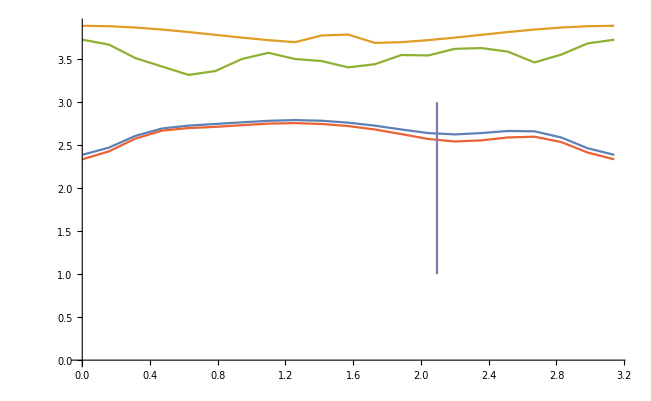

```mathematica
ListLinePlot[{rd32mean,rd32max,rd16max,rd16mean,{{2.0943951023931953,1},{2.0943951023931953,3}}}]
```

```mathematica
N[2Pi/3]
```

2.0944

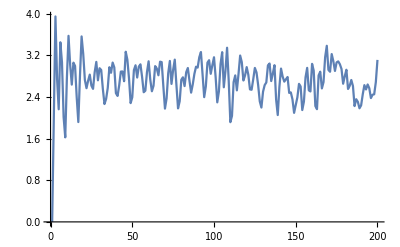

```mathematica
ListLinePlot[rd64n[[6]]]
```

## dt = pi/64

#### data

```mathematica
rd64={-0.000000000000000000*10^+00,2.000000000000000000*10^+00,3.972234460290947400*10^+00,2.226312826269990275*10^+00,6.442666605629060461*10^-01,2.171155130461605243*10^+00,3.794466733665000646*10^+00,2.395518351847664373*10^+00,1.124056318763379414*10^+00,2.357757913090019919*10^+00,3.692775718051163558*10^+00,2.669391251313184554*10^+00,1.782818610277733917*10^+00,2.368171617776035021*10^+00,3.232598640962807579*10^+00,2.425732283322516558*10^+00,1.385003977198919323*10^+00,2.479793548983265872*10^+00,3.615320906236606735*10^+00,2.581298017162434011*10^+00,1.889409568911662340*10^+00,2.487793089178919281*10^+00,3.394986106567748241*10^+00,2.801489135961738430*10^+00,2.128331065450590032*10^+00,2.196309357558596353*10^+00,2.796003156015806290*10^+00,2.681246266320277627*10^+00,1.688080722501665631*10^+00,2.287570241071511745*10^+00,3.202276978932509177*10^+00,2.661243027066238387*10^+00,1.725632663316345905*10^+00,2.069096156078668702*10^+00,2.879172054565724892*10^+00,2.724824630326948327*10^+00,2.065252721607058195*10^+00,2.039837338583355475*10^+00,2.783606436693875530*10^+00,2.416523798472264506*10^+00,1.609482597349379152*10^+00,1.958417738772101124*10^+00,2.706435106466284601*10^+00,2.309400716705633627*10^+00,1.733738228305293561*10^+00,2.268841536351517529*10^+00,2.522160301826585904*10^+00,2.570029962802766299*10^+00,2.283684783069033664*10^+00,2.139380760530615433*10^+00,2.607412189278095926*10^+00,2.653093144058281450*10^+00,1.902254731995530523*10^+00,1.769862352682032736*10^+00,2.341853720395294047*10^+00,2.729929100347536775*10^+00,2.217836569007295644*10^+00,2.039717375186066217*10^+00,2.620446609636785773*10^+00,2.593277296918016894*10^+00,2.218249941940181102*10^+00,1.836033945736257555*10^+00,2.179285921012816818*10^+00,2.415740183163995525*10^+00,2.286586436498410091*10^+00,2.165967982437650097*10^+00,2.341566998395467891*10^+00,2.424491988865511871*10^+00,2.157561433089293157*10^+00,2.035157236921590229*10^+00,2.385966341626165832*10^+00,2.691930587296310851*10^+00,2.317582241802727872*10^+00,1.928280053200105426*10^+00,2.391175961315898491*10^+00,2.885202103891516323*10^+00,2.533472918595699674*10^+00,2.143999295187600129*10^+00,2.640042358269461431*10^+00,2.831586763720912447*10^+00,2.316237390077989566*10^+00,2.030184740422715350*10^+00,2.599890016766472467*10^+00,2.570859942405236076*10^+00,2.168636439437991115*10^+00,2.158375256807544940*10^+00,2.683474351320467743*10^+00,2.799935678877269130*10^+00,2.528559328375949988*10^+00,2.564490461179963710*10^+00,2.948148806285239232*10^+00,2.905648317667024916*10^+00,2.505972514037207777*10^+00,2.494207063245787559*10^+00,2.714095232131816360*10^+00,2.679468832821764401*10^+00,2.558965818601898867*10^+00,2.600353410784550956*10^+00,2.672960029948173499*10^+00,2.460709582900062919*10^+00,2.180453659380245046*10^+00,2.453409224137162337*10^+00,2.854533270748525808*10^+00,2.615855709286149633*10^+00,2.064231715090859343*10^+00,2.230625902544737915*10^+00,2.755441620983471118*10^+00,2.469837711066652730*10^+00,1.694957090393133026*10^+00,1.992137649464228666*10^+00,2.995098020005544370*10^+00,2.530400914114466993*10^+00,1.729201564457856666*10^+00,2.204059720483436013*10^+00,2.853246457926088109*10^+00,2.559410159685370001*10^+00,2.360407361460416631*10^+00,2.449249529215552279*10^+00,2.832838841189546208*10^+00,2.577002254463636177*10^+00,2.448363149420077711*10^+00,2.306267808630272143*10^+00,2.549278733947811570*10^+00,2.380991287046221316*10^+00,2.131241013133353679*10^+00,2.148659475545970476*10^+00,2.995629637236350895*10^+00,2.798504312530762039*10^+00,2.179799019927940229*10^+00,2.238008225118348182*10^+00,2.714810570305196347*10^+00,2.721418670951559537*10^+00,2.598921292575153696*10^+00,2.477545458150181457*10^+00,2.816511806237596005*10^+00,2.945650524716445062*10^+00,2.511310736477968764*10^+00,2.084270989606460844*10^+00,2.556344808813906688*10^+00,2.614988334294030992*10^+00,2.137021152909185595*10^+00,1.716061034601291224*10^+00,2.365857956322356515*10^+00,2.579648018571996548*10^+00,2.273331362211355344*10^+00,1.833635685852365693*10^+00,2.538225124379805298*10^+00,2.665337224992207155*10^+00,1.969725873546189110*10^+00,1.883325829558295972*10^+00,2.597142259005857490*10^+00,2.559348966675353942*10^+00,1.725779058673978072*10^+00,1.822905620778093150*10^+00,2.665589041971739181*10^+00,2.669836461389689664*10^+00,1.964418145914794245*10^+00,2.064977275495508913*10^+00,2.912440873456241697*10^+00,2.666219114049419581*10^+00,1.612136827607085321*10^+00,1.713064318736760461*10^+00,2.821806298702250526*10^+00,2.760526890701602731*10^+00,1.890115538384116833*10^+00,1.988338488026855977*10^+00,2.864009330853313884*10^+00,2.974697066466894135*10^+00,2.204007374855338153*10^+00,2.298813916950609659*10^+00,3.088128300368135015*10^+00,3.320017756671451270*10^+00,2.646571372450287285*10^+00,2.432804233303107022*10^+00,3.143549684083241758*10^+00,3.193717489813012289*10^+00,2.429065281231649998*10^+00,2.392446345048260703*10^+00,3.029618388363916726*10^+00,2.715027805342164147*10^+00,1.867113965762443373*10^+00,1.997446023703076889*10^+00,2.874420629081782863*10^+00,2.654900192639523038*10^+00,1.792736361040155213*10^+00,1.538259517208707239*10^+00,2.508286376613163782*10^+00,2.708267157204056641*10^+00,2.164167092974234929*10^+00,1.887382999122367178*10^+00,2.404509217861504844*10^+00,2.982731352428527494*10^+00,1.819546866601659429*10^+00,1.644503464610457266*10^+00,2.476575804249524282*10^+00,2.945745044643184318*10^+00,2.097727640134968041*10^+00,1.367297603583751631*10^+00,2.341789817086298076*10^+00,3.343264196293304735*10^+00,2.722912528242654327*10^-14,1.999321645901668276*10^+00,3.970886869222546078*10^+00,2.475813923412640172*10^+00,9.344830299637936211*10^-01,2.435287013137991785*10^+00,3.693789305089111519*10^+00,2.388255868791109737*10^+00,1.165215524549189308*10^+00,2.354059255384929550*10^+00,3.670766065337308870*10^+00,2.859492961273256473*10^+00,2.019172443959160290*10^+00,2.578249240288247535*10^+00,3.210840215518415697*10^+00,2.443826946897438290*10^+00,1.439331982136056620*10^+00,2.531340653609590152*10^+00,3.648761823667770798*10^+00,2.774935300699292284*10^+00,2.094020531872991420*10^+00,2.580449849470668244*10^+00,3.312840577789606833*10^+00,2.806070574987975519*10^+00,2.194094852682601182*10^+00,2.275428992503994330*10^+00,2.873309059666598220*10^+00,2.863443581342318023*10^+00,1.946601979935274729*10^+00,2.483225854256280396*10^+00,3.163021433799505733*10^+00,2.702783955505499769*10^+00,1.817121826833284270*10^+00,2.082542638474656371*10^+00,2.809251678393437590*10^+00,2.783327965311864993*10^+00,2.265333809103712959*10^+00,2.187619694042828744*10^+00,2.797428549455116542*10^+00,2.459372607740784478*10^+00,1.723551202527491721*10^+00,2.030377159788325780*10^+00,2.685247644493584218*10^+00,2.382296827847818932*10^+00,1.922812634682815824*10^+00,2.417178848212833131*10^+00,2.555619985393090765*10^+00,2.586154814906444166*10^+00,2.268424287786314331*10^+00,2.154987754871803940*10^+00,2.604694732986721384*10^+00,2.725398274540793420*10^+00,2.109068037843834453*10^+00,1.932948495976483549*10^+00,2.352904277427576130*10^+00,2.712863251568288447*10^+00,2.244145319121697568*10^+00,2.105507248539324916*10^+00,2.651894531091273599*10^+00,2.739108589215311085*10^+00,2.355092736040396151*10^+00,1.940070501650454471*10^+00,2.165674667633725292*10^+00,2.472988488192972234*10^+00,2.405366212634904688*10^+00,2.319332594168723283*10^+00,2.462953699235006511*10^+00,2.551227334935822544*10^+00,2.284108199392405947*10^+00,2.095944057218791290*10^+00,2.352959651852236878*10^+00,2.705146708745335360*10^+00,2.475230041707537687*10^+00,2.107505993298546709*10^+00,2.521910750406828328*10^+00,2.932943369650512278*10^+00,2.627158101553204173*10^+00,2.208772408154788813*10^+00,2.592350841489308166*10^+00,2.769069502557672813*10^+00,2.337112066174517722*10^+00,2.129777956498825731*10^+00,2.660997192643948850*10^+00,2.686371458780399735*10^+00,2.329691386201706571*10^+00,2.309935312603168533*10^+00,2.653862314133207612*10^+00,2.755658141722919119*10^+00,2.551707588775448343*10^+00,2.677733949333616525*10^+00,3.003688088886124596*10^+00,2.955276204729555989*10^+00,2.612088580574485341*10^+00,2.534474119821830129*10^+00,2.649459163966497499*10^+00,2.680337121233359099*10^+00,2.680264228526146653*10^+00,2.765591217987508177*10^+00,2.779297263706265841*10^+00,2.570460122395409552*10^+00,2.275371402066848070*10^+00,2.492604371038241506*10^+00,2.799439506305324343*10^+00,2.645508086344640297*10^+00,2.269938283001177393*10^+00,2.408968728507461243*10^+00,2.841018187299871212*10^+00,2.619430214226240228*10^+00,1.898218993243436570*10^+00,2.104649854828635203*10^+00,2.905950411460735516*10^+00,2.540221880768182672*10^+00,1.890231972121941606*10^+00,2.300221504372193415*10^+00,2.882009681758514574*10^+00,2.648969551069452422*10^+00,2.487101606977861312*10^+00,2.560277211985916068*10^+00,2.844270789277630662*10^+00,2.597959706572951610*10^+00,2.510726671555322476*10^+00,2.403705255781625638*10^+00,2.584685059149824049*10^+00,2.472421752071943590*10^+00,2.307872500130018434*10^+00,2.313137130005664233*10^+00,3.002049653409706309*10^+00,2.778260415585700027*10^+00,2.161789706270725198*10^+00,2.262728162276903987*10^+00,2.704530439848533252*10^+00,2.775766852066623436*10^+00,2.731560523089611614*10^+00,2.632287826310367951*10^+00,2.895341194320749434*10^+00,2.950329493485472909*10^+00,2.546884444431136263*10^+00,2.110085870877450809*10^+00,2.488221874954996249*10^+00,2.652368141032424020*10^+00,2.281032686011582378*10^+00,1.930767456418508443*10^+00,2.448533600555701462*10^+00,2.579934885088409402*10^+00,2.345032827027812239*10^+00,1.932219758095135465*10^+00,2.572709267305793635*10^+00,2.649489043429060331*10^+00,2.105960432165788099*10^+00,2.054417534031488302*10^+00,2.620071669914542323*10^+00,2.558744029394822928*10^+00,1.809584549284140920*10^+00,1.868045744140855557*10^+00,2.627289783881584739*10^+00,2.696017584557202973*10^+00,2.118582281818650603*10^+00,2.255228048894390103*10^+00,2.986542496983122241*10^+00,2.684704511633650093*10^+00,1.732042834838697587*10^+00,1.798717108671313625*10^+00,2.770586344992489458*10^+00,2.811290126288679581*10^+00,2.096415794700882351*10^+00,2.218108002236233833*10^+00,2.998461579682804246*10^+00,2.985605720277391573*10^+00,2.306578077943549410*10^+00,2.357266128816905670*10^+00,3.067821628778206744*10^+00,3.327677068808796879*10^+00,2.796226554859481350*10^+00,2.623621417301812198*10^+00,3.192703877876135188*10^+00,3.176193206819928783*10^+00,2.503822053877065024*10^+00,2.459002665961413037*10^+00,3.010671145878488719*10^+00,2.756887711709802957*10^+00,2.078049273200067937*10^+00,2.188696274650731244*10^+00,2.914162409478100901*10^+00,2.635522269250096361*10^+00,1.836128513711632326*10^+00,1.597187889815148365*10^+00,2.499202948134540581*10^+00,2.681114943060908473*10^+00,2.237579520562586133*10^+00,2.017920366730578507*10^+00,2.484364626416971866*10^+00,2.962944629806700814*10^+00,1.942767892364864135*10^+00,1.778997989131618551*10^+00,2.520843448418749411*10^+00,2.906190903913911772*10^+00,2.227582985138246929*10^+00,1.571358114403054840*10^+00,2.436316522540784124*10^+00,3.342460446216412251*10^+00,-9.610279511444755881*10^-16,1.997353286798289496*10^+00,3.966980812630833686*10^+00,2.827593514006927489*10^+00,1.413558390924810837*10^+00,2.763908212783971585*10^+00,3.471025900019582000*10^+00,2.375087994812096870*10^+00,1.268884273348221958*10^+00,2.359319063320244325*10^+00,3.616671039003560573*10^+00,3.129047955229703692*10^+00,2.329138240331777965*10^+00,2.851604748852630156*10^+00,3.114671195997258835*10^+00,2.458622913603218940*10^+00,1.579300560090456385*10^+00,2.616980127686232560*10^+00,3.679066694954892025*10^+00,3.042497646073661244*10^+00,2.429191580681450802*10^+00,2.637587644494596262*10^+00,3.085809562683992979*10^+00,2.774811879260579595*10^+00,2.341162593853835627*10^+00,2.390272464644837225*10^+00,2.928615573899068458*10^+00,3.096488361860699090*10^+00,2.325804690647584660*10^+00,2.711983811262845379*10^+00,3.079638933041383808*10^+00,2.748257390831176483*10^+00,2.011013564301256551*10^+00,2.123437785228774022*10^+00,2.664724432247571162*10^+00,2.903592183029416685*10^+00,2.536836908636349808*10^+00,2.417189361070908316*10^+00,2.858438259073876608*10^+00,2.529837100194358257*10^+00,1.987147465282279590*10^+00,2.181961884717991573*10^+00,2.630395887135898114*10^+00,2.544504355884257940*10^+00,2.223392783532505135*10^+00,2.650129526446678874*10^+00,2.684953322608522264*10^+00,2.626056378674352487*10^+00,2.259586219901272841*10^+00,2.179120002958065072*10^+00,2.587094820242096915*10^+00,2.844357637945363670*10^+00,2.401047051717246639*10^+00,2.254900761590741265*10^+00,2.377591011348624939*10^+00,2.665471251211299908*10^+00,2.312759274093897144*10^+00,2.236377181765371702*10^+00,2.709648429431979366*10^+00,2.954450777065338762*10^+00,2.613864642858118259*10^+00,2.117926125848184959*10^+00,2.139470211911187469*10^+00,2.600394303112830041*10^+00,2.651350838293034418*10^+00,2.538758704510421627*10^+00,2.644858393296872112*10^+00,2.800642397012212736*10^+00,2.515597922174841905*10^+00,2.164087586701660015*10^+00,2.266662716657606325*10^+00,2.743938495321685878*10^+00,2.778961622546089139*10^+00,2.386245278971873329*10^+00,2.696305162878412709*10^+00,3.081998156357871554*10^+00,2.779889157874690042*10^+00,2.287995718814365365*10^+00,2.461319554391275588*10^+00,2.664683166948172754*10^+00,2.399344756514973476*10^+00,2.295740751605333418*10^+00,2.777695300729282391*10^+00,2.884495898702308825*10^+00,2.550989369327224754*10^+00,2.494145219113713896*10^+00,2.573348581877933139*10^+00,2.665263031090039370*10^+00,2.631511429916499445*10^+00,2.841293152581832349*10^+00,3.124262375592348207*10^+00,3.099409158367478323*10^+00,2.797822234347355774*10^+00,2.592239709172612372*10^+00,2.527084367259798015*10^+00,2.716197876231216224*10^+00,2.930995822590603428*10^+00,2.954841162315756442*10^+00,2.874842029126205567*10^+00,2.835873265004523081*10^+00,2.481645508772873931*10^+00,2.514277599666828067*10^+00,2.672808162337243054*10^+00,2.725094680860769447*10^+00,2.703185640531032607*10^+00,2.643723716328484130*10^+00,2.922991755097361199*10^+00,2.903342056237754321*10^+00,2.252467403633696019*10^+00,2.214279971783874146*10^+00,2.680176803845585543*10^+00,2.525840187122276426*10^+00,2.200099411756869738*10^+00,2.468105501181771633*10^+00,2.925227646205691201*10^+00,2.855677346673481942*10^+00,2.731637643896664969*10^+00,2.710526109137686213*10^+00,2.815297296951447148*10^+00,2.608371411669734741*10^+00,2.643471112468417150*10^+00,2.564204632722954180*10^+00,2.616154019032096656*10^+00,2.598460116115989482*10^+00,2.620035420121864966*10^+00,2.608287509828785655*10^+00,2.995833808494027473*10^+00,2.668773656214801449*10^+00,2.103576140651671977*10^+00,2.310457242482090834*10^+00,2.665936930136792782*10^+00,2.780551422974851583*10^+00,2.949469332338627403*10^+00,2.884498524295262101*10^+00,2.975452811506786421*10^+00,2.886593136992182451*10^+00,2.621266087979111870*10^+00,2.167412034367236728*10^+00,2.323083725866543325*10^+00,2.689983666379654803*10^+00,2.595635932081472141*10^+00,2.340551073729312037*10^+00,2.564565751761063606*10^+00,2.572842886267798779*10^+00,2.470259021367322116*10^+00,2.134225197593543122*10^+00,2.588875021739570848*10^+00,2.635535618285295811*10^+00,2.329336282570038552*10^+00,2.356306965911683982*10^+00,2.651474430567941187*10^+00,2.523192790793939100*10^+00,2.003451953442158207*10^+00,1.944690408155031802*10^+00,2.533934072652733072*10^+00,2.730261129212707694*10^+00,2.468391056967514263*10^+00,2.549945236346472743*10^+00,3.047304921414673906*10^+00,2.701058274247810864*10^+00,2.026677904649102580*10^+00,1.950515209948248785*10^+00,2.609444660683274186*10^+00,2.855615836401737884*10^+00,2.498521137416125359*10^+00,2.558614508772186991*10^+00,3.092886530313642357*10^+00,3.001887150651920688*10^+00,2.558697204282804893*10^+00,2.501430652671268628*10^+00,2.999701219050523893*10^+00,3.327806661713519354*10^+00,3.072803767599634917*10^+00,2.924391571464641348*10^+00,3.296505332906001673*10^+00,3.147307366294664455*10^+00,2.648130337491662711*10^+00,2.636937925854161868*10^+00,2.952035303780727205*10^+00,2.834486684384868393*10^+00,2.472254049204550164*10^+00,2.520746819665832916*10^+00,2.957633179530968270*10^+00,2.582399759145372897*10^+00,1.978370251151582160*10^+00,1.753835393826741917*10^+00,2.463127680578230283*10^+00,2.599450224626524086*10^+00,2.360032320918309168*10^+00,2.301136395655967171*10^+00,2.618020688816949715*10^+00,2.924379640752208687*10^+00,2.150725562405282343*10^+00,2.054758202290561719*10^+00,2.589226592259484594*10^+00,2.831107021380784960*10^+00,2.454244250759634483*10^+00,1.940293186774961542*10^+00,2.572110527684964509*10^+00,3.324092937078130916*10^+00,9.610279511444749964*10^-16,1.994288388562598824*10^+00,3.960908447015873524*10^+00,2.993811126825866697*10^+00,1.791934672090820246*10^+00,3.015639899506587174*10^+00,3.267006071134518574*10^+00,2.311561399011027973*10^+00,1.407599558615552748*10^+00,2.412457426759614165*10^+00,3.567916228322573602*10^+00,3.233364890344033071*10^+00,2.521203300135527847*10^+00,2.977925457335054205*10^+00,2.966909204292361935*10^+00,2.439803849032528227*10^+00,1.715450782241968231*10^+00,2.668861973378966468*10^+00,3.649787335733853055*10^+00,3.213231397229758812*10^+00,2.645379352897241798*10^+00,2.578288652295488426*10^+00,2.800347937361736150*10^+00,2.780614960643944755*10^+00,2.472811834670797015*10^+00,2.448951385127084102*10^+00,2.905239367791997651*10^+00,3.189267601911351946*10^+00,2.584873285410642652*10^+00,2.833739622607179154*10^+00,2.987543368015043388*10^+00,2.729552916703031240*10^+00,2.199216208720813359*10^+00,2.185748412656033590*10^+00,2.524188099456408541*10^+00,2.944131716219245298*10^+00,2.696879226704936627*10^+00,2.627256987322292847*10^+00,2.868548962840260064*10^+00,2.553449508804636725*10^+00,2.241818080946195835*10^+00,2.363774534152798701*10^+00,2.600858513331115507*10^+00,2.687790940774447801*10^+00,2.454370227527277848*10^+00,2.884351692813839740*10^+00,2.887709226321170775*10^+00,2.686268143623012694*10^+00,2.251639737375461969*10^+00,2.225587999333576761*10^+00,2.595114940897384148*10^+00,2.921116988825913641*10^+00,2.619491574671396705*10^+00,2.533776903498106137*10^+00,2.468466555196072942*10^+00,2.652758798485588265*10^+00,2.405101628960358617*10^+00,2.337434793448653902*10^+00,2.734865626590287757*10^+00,3.099050086891376843*10^+00,2.775530185199674538*10^+00,2.256144122673680918*10^+00,2.207468785851668613*10^+00,2.757556860491275685*10^+00,2.845772531756517232*10^+00,2.678940965219196890*10^+00,2.821067380808509828*10^+00,3.006534988150439514*10^+00,2.663740480472777783*10^+00,2.160012393603665259*10^+00,2.211975419620725969*10^+00,2.796770020613219110*10^+00,2.997892179375036825*10^+00,2.553687501434797280*10^+00,2.797862232658656634*10^+00,3.204078126641960900*10^+00,2.831208564573234554*10^+00,2.271332410209922159*10^+00,2.345094196468612502*10^+00,2.626809703727501333*10^+00,2.489001970527923380*10^+00,2.429924689833083740*10^+00,2.859877740132636958*10^+00,2.980702483624169119*10^+00,2.660394962152981879*10^+00,2.540082726665590762*10^+00,2.511689895503084635*10^+00,2.646897418376243483*10^+00,2.733772969371394801*10^+00,2.932610016673975917*10^+00,3.173642685256561791*10^+00,3.235034344919267113*10^+00,2.918495918024140767*10^+00,2.555580146330809654*10^+00,2.421740271592397242*10^+00,2.802318623729198155*10^+00,3.117367108158123568*10^+00,2.996940157214260214*10^+00,2.918281765179167042*10^+00,3.058709126030852765*10^+00,2.682201997992554432*10^+00,2.472248014951020867*10^+00,2.509247125672773304*10^+00,2.837799218596214423*10^+00,3.049785043587441180*10^+00,2.721937268396382947*10^+00,2.887851850548034172*10^+00,3.146297323617814445*10^+00,2.542203669476301719*10^+00,2.173656772353699917*10^+00,2.327056048798534782*10^+00,2.495184044692258851*10^+00,2.485062869861199619*10^+00,2.542818344278026998*10^+00,2.897570431976193017*10^+00,3.053003217892791721*10^+00,2.954491490936495879*10^+00,2.758723085681465736*10^+00,2.684590331140369823*10^+00,2.625408192168440458*10^+00,2.754759338498108612*10^+00,2.630376760018199533*10^+00,2.579661776026293207*10^+00,2.657470197952763069*10^+00,2.848466699628797727*10^+00,2.798522162174766237*10^+00,2.879353500165002799*10^+00,2.478054941686957946*10^+00,2.043984434830221630*10^+00,2.361719065784601668*10^+00,2.649256741451903263*10^+00,2.724978352089715283*10^+00,3.099608165864327081*10^+00,3.060652375991667284*10^+00,2.918782267921465667*10^+00,2.801077168723622002*10^+00,2.706203952085874942*10^+00,2.221926744739494808*10^+00,2.152972500988854065*10^+00,2.638974043333059516*10^+00,2.866340526730423388*10^+00,2.646978022689276067*10^+00,2.614041760615705812*10^+00,2.572015748081388331*10^+00,2.601557981688431109*10^+00,2.295705530077691403*10^+00,2.559776934047395258*10^+00,2.555435158471250467*10^+00,2.412964568719041303*10^+00,2.513803714712199877*10^+00,2.601468311082976825*10^+00,2.559184391798826841*10^+00,2.217281547760298288*10^+00,2.003856056851368805*10^+00,2.405462609481400449*10^+00,2.743146428845548712*10^+00,2.782982672544918490*10^+00,2.718990643810977659*10^+00,2.940183496497195570*10^+00,2.749923319908546659*10^+00,2.347259449593531944*10^+00,2.101392159319245945*10^+00,2.380100525481623208*10^+00,2.843489610450096183*10^+00,2.814154896399160055*10^+00,2.762054227494975756*10^+00,3.018933271346288638*10^+00,3.012538682642180277*10^+00,2.875833191527770616*10^+00,2.664647630048472937*10^+00,2.886376832293126693*10^+00,3.275014430033132307*10^+00,3.229190918430139945*10^+00,3.103367703155126112*10^+00,3.292870185697007290*10^+00,3.086606884781113891*10^+00,2.780166221920479686*10^+00,2.763108205543844065*10^+00,2.814047865747525634*10^+00,2.838422374927893177*10^+00,2.796408817936206770*10^+00,2.731558081306092234*10^+00,2.931149057524320867*10^+00,2.573123646408579823*10^+00,2.164680994242636380*10^+00,1.924809096181250956*10^+00,2.416111282703612861*10^+00,2.477962236183795852*10^+00,2.396172472046727897*10^+00,2.451437004996909419*10^+00,2.663966021357871750*10^+00,2.843876742075994724*10^+00,2.338493955639992183*10^+00,2.343492442417184130*10^+00,2.640821498669626344*10^+00,2.718739539714980502*10^+00,2.587305425197374831*10^+00,2.237783687031407176*10^+00,2.651569058535507395*10^+00,3.271261507355187614*10^+00,4.805139755722374982*10^-16,1.990427942067828582*10^+00,3.953269517893640561*10^+00,2.950067639789189844*10^+00,2.043908100128757344*10^+00,3.220635790229778195*10^+00,3.128338209574795137*10^+00,2.186053828949563904*10^+00,1.530243259938147915*10^+00,2.575880326273332521*10^+00,3.561033234535731840*10^+00,3.164172233603109952*10^+00,2.606760477033637002*10^+00,3.011057134220331388*10^+00,2.915882405733721594*10^+00,2.418544276922706349*10^+00,1.828208447173887086*10^+00,2.718893994481031307*10^+00,3.595107842943474186*10^+00,3.257251388042980533*10^+00,2.726049056497808820*10^+00,2.526585537043493979*10^+00,2.677701529005277692*10^+00,2.799466729593760306*10^+00,2.569869490013432234*10^+00,2.485977300612501661*10^+00,2.855763349999097755*10^+00,3.152703752886566679*10^+00,2.695476015392058056*10^+00,2.871334272608321747*10^+00,2.912897337206389992*10^+00,2.642584023056723463*10^+00,2.297109688997099219*10^+00,2.283298325402135731*10^+00,2.500455748236777076*10^+00,2.960816167860861547*10^+00,2.798514313824198574*10^+00,2.835541190200657091*10^+00,2.886301710005355847*10^+00,2.520969770864030846*10^+00,2.388992922800325047*10^+00,2.506389934265885078*10^+00,2.682563371413227316*10^+00,2.802367939497852234*10^+00,2.594574742504377696*10^+00,3.075009952268355384*10^+00,3.052954521679535738*10^+00,2.726495685875666375*10^+00,2.244408239074250133*10^+00,2.297261541377556782*10^+00,2.713901277074077356*10^+00,2.987645493712480338*10^+00,2.725974736374262353*10^+00,2.761173222606742250*10^+00,2.735552397747676334*10^+00,2.704329401700076740*10^+00,2.468205126378652636*10^+00,2.425153652222880041*10^+00,2.800321963394802438*10^+00,3.137727653650377313*10^+00,2.795803502841530896*10^+00,2.361190600752253399*10^+00,2.397394344192902871*10^+00,2.903365116190210315*10^+00,2.933309951285498318*10^+00,2.743252451309380113*10^+00,2.970285834884346166*10^+00,3.093071936462712834*10^+00,2.673466654068900716*10^+00,2.125351437423223189*10^+00,2.285105270475145556*10^+00,2.833855805261733085*10^+00,3.090088184958444728*10^+00,2.616158941048315700*10^+00,2.870146001262954272*10^+00,3.208094403516792870*10^+00,2.749909799191203597*10^+00,2.203204728875045593*10^+00,2.289803352043556117*10^+00,2.655134010002095479*10^+00,2.620632902023377397*10^+00,2.519925454199460457*10^+00,2.885039842364476748*10^+00,2.999360879545869274*10^+00,2.693508983598947637*10^+00,2.506917682469511632*10^+00,2.530615321778767246*10^+00,2.707990751253223749*10^+00,2.847594741452746270*10^+00,2.949294376307562082*10^+00,3.178775518771528308*10^+00,3.290114246026982769*10^+00,2.917756982632539575*10^+00,2.457304321692892923*10^+00,2.455417821712091886*10^+00,2.925876060346908503*10^+00,3.162843261010162887*10^+00,2.919544574896022926*10^+00,2.964739791124422652*10^+00,3.167018012152079454*10^+00,2.781868267821629992*10^+00,2.372683386839648634*10^+00,2.450999056293323708*10^+00,2.957250303307585426*10^+00,3.226239751976427428*10^+00,2.665058822927188764*10^+00,2.860258403470719912*10^+00,3.290273786317665650*10^+00,2.684213609153661029*10^+00,2.038174080853409009*10^+00,2.045856098176472404*10^+00,2.532557529487184489*10^+00,2.682050613391934846*10^+00,2.541938606907762299*10^+00,2.853915182307404486*10^+00,3.172567106408066717*10^+00,3.062806161574406882*10^+00,2.729298604544630358*10^+00,2.623551743477349429*10^+00,2.752651770408106380*10^+00,2.794188383316490665*10^+00,2.604433332101225407*10^+00,2.558993004703365326*10^+00,2.698536813132642820*10^+00,2.947225053640583070*10^+00,2.868959383942392360*10^+00,2.724868025327476850*10^+00,2.310904161642428623*10^+00,2.054478409043687837*10^+00,2.409029504983744907*10^+00,2.622169701172687439*10^+00,2.664496956971345920*10^+00,3.112472388112396793*10^+00,3.098209968479784138*10^+00,2.803826700571464325*10^+00,2.783969224715309387*10^+00,2.850159560136062531*10^+00,2.275995279602686328*10^+00,2.051572911040286051*10^+00,2.581053111889120011*10^+00,2.978278012121938545*10^+00,2.782247122011820117*10^+00,2.644683053280613372*10^+00,2.635767011284333883*10^+00,2.712333786800626978*10^+00,2.402402808093208275*10^+00,2.508097049590056749*10^+00,2.454158933136534770*10^+00,2.311471801921241020*10^+00,2.439599872527861368*10^+00,2.497163685584593562*10^+00,2.615459893251673051*10^+00,2.431943774884811393*10^+00,2.073469785626202544*10^+00,2.311913585730065446*10^+00,2.748819542044446784*10^+00,2.954097177420199838*10^+00,2.695482075196929284*10^+00,2.736199473182372888*10^+00,2.859665440151810678*10^+00,2.648556345228082698*10^+00,2.188882149182969972*10^+00,2.190075820910790227*10^+00,2.794653653819229255*10^+00,2.933690043051453422*10^+00,2.747986020968810728*10^+00,2.847524862787040867*10^+00,3.062252377190327390*10^+00,3.173381318610037471*10^+00,2.825227210621040541*10^+00,2.811369846418157348*10^+00,3.204625746507064221*10^+00,3.182628347518589251*10^+00,3.062781622663114156*10^+00,3.194378067549121347*10^+00,3.068969115727913977*10^+00,2.896118028741201389*10^+00,2.848719651350558824*10^+00,2.680596447776306679*10^+00,2.797887045949499107*10^+00,2.941565000777820682*10^+00,2.739488058724315778*10^+00,2.798927116075719645*10^+00,2.619552868634979603*10^+00,2.392026816531693356*10^+00,2.082784856325817557*10^+00,2.368538793710031509*10^+00,2.357508466619333998*10^+00,2.304945549798218973*10^+00,2.401057167364873735*10^+00,2.593245301180821194*10^+00,2.737113233697426651*10^+00,2.465288692117061586*10^+00,2.547291163960745841*10^+00,2.630830129504452497*10^+00,2.569503842997885368*10^+00,2.574001313971400862*10^+00,2.405240386831255517*10^+00,2.676349534995574153*10^+00,3.180728153368329814*10^+00,3.203426503814917641*10^-16,1.986150627926013046*10^+00,3.944807183751711133*10^+00,2.745309522276101255*10^+00,2.162575161256696354*10^+00,3.449034045603885268*10^+00,3.064548455996040754*10^+00,2.013283289589136604*10^+00,1.623502869054454179*10^+00,2.759757731213749565*10^+00,3.572809343717793240*10^+00,3.018041795704903940*10^+00,2.635909695154119881*10^+00,3.057996500418066699*10^+00,2.994582724800680218*10^+00,2.398436882890726096*10^+00,1.917077786982895660*10^+00,2.799319263210521491*10^+00,3.561420014647202592*10^+00,3.224113496867194506*10^+00,2.726414564078718072*10^+00,2.567637666985562284*10^+00,2.711947617516331732*10^+00,2.827521888909673820*10^+00,2.617278206462421153*10^+00,2.554431140227583885*10^+00,2.874390301946427861*10^+00,3.072418252187050669*10^+00,2.718761912434889183*10^+00,2.950872241717831912*10^+00,2.917120788215663119*10^+00,2.554655054890983656*10^+00,2.263460752889609573*10^+00,2.361036405442160646*10^+00,2.572040456233306571*10^+00,2.969828480544254301*10^+00,2.862662394908036312*10^+00,3.059573090510424365*10^+00,2.967093307415074932*10^+00,2.471824669635843907*10^+00,2.418591517674773428*10^+00,2.621686861289523218*10^+00,2.885877891604221368*10^+00,2.888741763926089057*10^+00,2.701411305748453895*10^+00,3.267194941891421678*10^+00,3.114837723298836902*10^+00,2.756686282278691280*10^+00,2.281022783580723967*10^+00,2.393020999382332370*10^+00,2.914253313375521959*10^+00,3.007727646458755455*10^+00,2.772120488023006146*10^+00,2.980980506565082511*10^+00,3.025602606289236274*10^+00,2.785725654369056947*10^+00,2.489944836958392305*10^+00,2.518865333116389493*10^+00,2.877106249041747166*10^+00,3.084063348751334921*10^+00,2.735124324726780465*10^+00,2.508171532892763178*10^+00,2.613844459340104898*10^+00,2.991543590046010337*10^+00,2.945487701148928217*10^+00,2.815728295247638790*10^+00,3.076641011433570050*10^+00,3.068040754313962726*10^+00,2.610886747417973552*10^+00,2.175112007635707556*10^+00,2.372795431098492447*10^+00,2.857898183144153670*10^+00,3.090640856360519440*10^+00,2.649523653284659108*10^+00,2.919813752197359058*10^+00,3.115874840123786349*10^+00,2.634947602750199458*10^+00,2.179916280906451842*10^+00,2.314906798116579179*10^+00,2.729597957707174505*10^+00,2.776385315718377100*10^+00,2.607884670091671353*10^+00,2.873719171738103650*10^+00,2.955339032166351299*10^+00,2.710152460008770525*10^+00,2.482226711546432263*10^+00,2.639920931113687530*10^+00,2.841662365380654087*10^+00,2.979237219880309873*10^+00,2.962811837631680767*10^+00,3.162219087604330348*10^+00,3.261477853874060973*10^+00,2.834370634201243355*10^+00,2.395280711543953167*10^+00,2.600892033618070087*10^+00,3.058091373845240213*10^+00,3.105033743838363502*10^+00,2.843674068407099575*10^+00,3.010852167716437044*10^+00,3.161148547039394519*10^+00,2.781367396452996132*10^+00,2.295516421342579161*10^+00,2.506027941940575321*10^+00,3.031656381261186972*10^+00,3.259102376317082328*10^+00,2.584898915810310172*10^+00,2.896388492137912163*10^+00,3.344216625910308771*10^+00,2.711961698561875966*10^+00,1.914790406332802730*10^+00,2.035413816894479755*10^+00,2.684097421501516756*10^+00,2.812724800975468398*10^+00,2.525667872316578855*10^+00,2.841763574078262078*10^+00,3.194380303524970266*10^+00,3.067263706575748206*10^+00,2.715847846600799365*10^+00,2.813712702336134797*10^+00,2.971947795307152695*10^+00,2.825053532064591977*10^+00,2.544977223324641269*10^+00,2.537174439781869850*10^+00,2.738301090875173482*10^+00,2.956698400931332404*10^+00,2.870288181151760654*10^+00,2.630783578861863425*10^+00,2.315228196143831241*10^+00,2.195843791385893251*10^+00,2.499697576954518219*10^+00,2.626649486032248682*10^+00,2.677625356856220940*10^+00,3.006172937787979116*10^+00,3.041430926973555771*10^+00,2.704584684300628261*10^+00,2.850055361153246203*10^+00,3.009048502302964057*10^+00,2.349750703229528614*10^+00,2.051639416609615019*10^+00,2.589602964472452751*10^+00,2.944135434521244488*10^+00,2.790128100901145380*10^+00,2.693238125843963715*10^+00,2.738099504049260169*10^+00,2.782349776645322681*10^+00,2.476049150662188669*10^+00,2.486384270002983676*10^+00,2.353595652547517236*10^+00,2.093898383206100000*10^+00,2.243326135354668960*10^+00,2.390530490517716267*10^+00,2.650802589352450056*10^+00,2.599748080746682621*10^+00,2.147669956036879935*10^+00,2.308230694073479583*10^+00,2.776637248815085890*10^+00,2.957621412180938769*10^+00,2.526311869411836497*10^+00,2.505102518683010260*10^+00,3.034523475736042197*10^+00,2.904407332989560331*10^+00,2.225174008294681816*10^+00,2.164232605019464906*10^+00,2.813261537041302329*10^+00,2.884344018551053157*10^+00,2.563077290730739755*10^+00,2.683882897574003223*10^+00,3.164482049782157969*10^+00,3.381668113926665331*10^+00,2.919227377932894996*10^+00,2.883057511618571045*10^+00,3.222681872191863306*10^+00,3.086726067677845187*10^+00,2.898793625761528769*10^+00,3.062423673935341206*10^+00,3.082092430450921849*10^+00,3.027786790950464102*10^+00,2.937280092035623902*10^+00,2.653189423222088728*10^+00,2.795289887278123331*10^+00,2.921186990862548516*10^+00,2.552358155841288223*10^+00,2.611839609924144323*10^+00,2.725256866220553409*10^+00,2.609262496956635591*10^+00,2.224304522420406993*10^+00,2.355486288362961034*10^+00,2.305741866501220372*10^+00,2.181475045820895797*10^+00,2.237248902351223201*10^+00,2.448744410858113341*10^+00,2.626349974925084929*10^+00,2.543007588907483019*10^+00,2.638979303816702426*10^+00,2.566931413955154451*10^+00,2.377586813007017241*10^+00,2.441788769449422247*10^+00,2.450602818059033794*10^+00,2.684076829727378488*10^+00,3.110493522064318395*10^+00,-9.610279511444755881*10^-16,1.981875445374428280*10^+00,3.936338717287444666*10^+00,2.543005131491850257*10^+00,2.208236412769727153*10^+00,3.659672230306577401*10^+00,3.043131258045002951*10^+00,1.878453183358502532*10^+00,1.664740336415638122*10^+00,2.880393886139844817*10^+00,3.560922553212742425*10^+00,2.874480331251216381*10^+00,2.643053849806080713*10^+00,3.218259103457925097*10^+00,3.084254788107521961*10^+00,2.356324920885492613*10^+00,1.997141104427460512*10^+00,2.908930514192149985*10^+00,3.549551066753192430*10^+00,3.139956863625391836*10^+00,2.738625833575917490*10^+00,2.796249640935941638*10^+00,2.791443350742116358*10^+00,2.803703363801417936*10^+00,2.606779737630523730*10^+00,2.616055928745227632*10^+00,2.953744065184630951*10^+00,3.002742095055554561*10^+00,2.728073765355168767*10^+00,3.078186106641161324*10^+00,2.942821783657824763*10^+00,2.459792201510902387*10^+00,2.135393148077006309*10^+00,2.370593807874717740*10^+00,2.735470367801652980*10^+00,2.989118994999206969*10^+00,2.933511081085150352*10^+00,3.288647803773753431*10^+00,2.971413698824282523*10^+00,2.440531349130294458*10^+00,2.386109381883840808*10^+00,2.728784463240830238*10^+00,3.116473689490022903*10^+00,2.982494668350340383*10^+00,2.800165197627545233*10^+00,3.442689081824692909*10^+00,3.099554220394145965*10^+00,2.771312135240342478*10^+00,2.351447756449105420*10^+00,2.511496047308225954*10^+00,3.115389698222364334*10^+00,3.034447683052980960*10^+00,2.804405199244580871*10^+00,3.136872172430795747*10^+00,3.200446402333338991*10^+00,2.818377134668183182*10^+00,2.496761333630564739*10^+00,2.565929426834933746*10^+00,2.900225825522816603*10^+00,2.971330177039821496*10^+00,2.673316620873996019*10^+00,2.699627501420393649*10^+00,2.783732544725761482*10^+00,3.011808815318877119*10^+00,2.951373572878204676*10^+00,2.911181157745931891*10^+00,3.121613929914409002*10^+00,2.990796867243952661*10^+00,2.574308318718684596*10^+00,2.298376083181199014*10^+00,2.441068083761218865*10^+00,2.837962982913174947*10^+00,3.067862129634075785*10^+00,2.693188982379076002*10^+00,2.918015006491855967*10^+00,2.987312466358110541*10^+00,2.563813235086477071*10^+00,2.259645539368802858*10^+00,2.379180405776330165*10^+00,2.783387575420689153*10^+00,2.917774375315221214*10^+00,2.736008065827339131*10^+00,2.863025176179952780*10^+00,2.897539388267051930*10^+00,2.755353149657398415*10^+00,2.524047651243409351*10^+00,2.721840970910625934*10^+00,2.972771409126390374*10^+00,3.127504490404208415*10^+00,3.002756276719844131*10^+00,3.141742852128524888*10^+00,3.185320868660772131*10^+00,2.727286157778711750*10^+00,2.439674488250543227*10^+00,2.722152079409287495*10^+00,3.157598984602345560*10^+00,3.070632066357869672*10^+00,2.831510943085397525*10^+00,3.015396402765592399*10^+00,3.137069414069909801*10^+00,2.735483082020205625*10^+00,2.287827634963930379*10^+00,2.582210922892449467*10^+00,3.061740675666782430*10^+00,3.228023235950216119*10^+00,2.551476913450878570*10^+00,2.929180388127627044*10^+00,3.340086326433114206*10^+00,2.695727124052996970*10^+00,1.889194690633474671*10^+00,2.191013714514992827*10^+00,2.857433261555272441*10^+00,2.918776691205585028*10^+00,2.533938390221277537*10^+00,2.829289606313126093*10^+00,3.188686560090742361*10^+00,3.000131269481538521*10^+00,2.768450824222858486*10^+00,3.016907855048604592*10^+00,3.160509581833376380*10^+00,2.871308416881658498*10^+00,2.492430758890198383*10^+00,2.481487300784614547*10^+00,2.723921545094812657*10^+00,2.902935657705168815*10^+00,2.871028610140220927*10^+00,2.676381477685706667*10^+00,2.446639365883081396*10^+00,2.387726283999949572*10^+00,2.595749425983395753*10^+00,2.631616767771377319*10^+00,2.694086477667784862*10^+00,2.849496655280272073*10^+00,2.944980878111674194*10^+00,2.722855551981193223*10^+00,2.982915293405101309*10^+00,3.115564867673692895*10^+00,2.402750494883182597*10^+00,2.186397816018460727*10^+00,2.635008768308858773*10^+00,2.813181086295199140*10^+00,2.729829038928146101*10^+00,2.727460157785251305*10^+00,2.782286325671243787*10^+00,2.826193806293223254*10^+00,2.515305452639482464*10^+00,2.501255998208058884*10^+00,2.308532742514590286*10^+00,1.919388406715946793*10^+00,2.094639117358402913*10^+00,2.300572138849557469*10^+00,2.597145489519657957*10^+00,2.718573705764079307*10^+00,2.235706354106877569*10^+00,2.362564225152137709*10^+00,2.838390930810031687*10^+00,2.836988990804657718*10^+00,2.304044125764401763*10^+00,2.356865868573116973*10^+00,3.128410945978700397*10^+00,3.094629129870169137*10^+00,2.220683893224009609*10^+00,2.299158350993322664*10^+00,2.914687625328463927*10^+00,2.774292217220699186*10^+00,2.326079652739927450*10^+00,2.593107212987269428*10^+00,3.230332284423091949*10^+00,3.499476205472505708*10^+00,2.965105375847676861*10^+00,3.012053653783025808*10^+00,3.370954091813277209*10^+00,3.145112051493726746*10^+00,2.761149146365473594*10^+00,2.937552352220126561*10^+00,3.113845968124757668*10^+00,3.131021748540633087*10^+00,3.038589429584970247*10^+00,2.776602051083789213*10^+00,2.875494223318239673*10^+00,2.810408706917145061*10^+00,2.285848756951301741*10^+00,2.400992936699722247*10^+00,2.755761874211303031*10^+00,2.780404364074098744*10^+00,2.355337636537507606*10^+00,2.398750299409952547*10^+00,2.353198629715661294*10^+00,2.111105170755574800*10^+00,2.082720838222455129*10^+00,2.310056431690524104*10^+00,2.559086936583483407*10^+00,2.613594439943887515*10^+00,2.640891227358808102*10^+00,2.459700320650092031*10^+00,2.245629623653460527*10^+00,2.284824936692928965*10^+00,2.468612778402123009*10^+00,2.746447365437924226*10^+00,3.030711468006146880*10^+00,-3.203426503814917641*10^-16,1.978020579463648954*10^+00,3.928684636842169287*10^+00,2.369372516907831017*10^+00,2.228269799104968474*10^+00,3.803831452449391470*10^+00,3.050607017789232600*10^+00,1.762370583930885637*10^+00,1.651252232718322999*10^+00,2.896259915704640697*10^+00,3.531554643986516862*10^+00,2.775223556761426291*10^+00,2.636362293658244482*10^+00,3.345311826043020353*10^+00,3.089605885516552686*10^+00,2.231724895106886208*10^+00,2.019728647358937756*10^+00,2.985220403791801758*10^+00,3.529520728919293582*10^+00,3.030439956871413987*10^+00,2.793901726384189210*10^+00,3.024388339813417481*10^+00,2.815268921647783529*10^+00,2.715067659297162095*10^+00,2.554275895595339296*10^+00,2.655194975412189962*10^+00,3.039215441280998409*10^+00,2.955173162717146251*10^+00,2.743123725772814492*10^+00,3.166269708702871277*10^+00,2.851343723018843868*10^+00,2.339253086217897071*10^+00,1.974922775957215437*10^+00,2.312128354311924205*10^+00,2.901019984965673260*10^+00,3.032609249340860735*10^+00,2.961261004553192855*10^+00,3.428591469628240684*10^+00,2.890969564188642593*10^+00,2.457438638358776295*10^+00,2.348589695023134638*10^+00,2.794037063975224111*10^+00,3.266710741485473690*10^+00,3.061433688581521650*10^+00,2.898794844875759669*10^+00,3.555771603754667165*10^+00,3.077046536827021672*10^+00,2.770805771525431282*10^+00,2.417035733438311240*10^+00,2.586745752229984152*10^+00,3.269920068537019109*10^+00,3.060748949375492689*10^+00,2.812928865538416368*10^+00,3.202866879026000202*10^+00,3.165094300405753458*10^+00,2.765979370855478070*10^+00,2.459473583674779640*10^+00,2.550827511938600800*10^+00,2.881908344889700935*10^+00,2.850633300524244351*10^+00,2.650754943025616317*10^+00,2.861085349166267555*10^+00,2.846922002128853713*10^+00,2.974731529937375107*10^+00,2.984926284739221281*10^+00,3.017428518494939205*10^+00,3.095820665287280171*10^+00,2.890159801935107797*10^+00,2.601184336373301598*10^+00,2.440674475056327175*10^+00,2.446484953382006999*10^+00,2.815658561028260287*10^+00,3.089895887416745701*10^+00,2.752048652056658717*10^+00,2.866615058201256616*10^+00,2.875195490745491078*10^+00,2.589008205861876633*10^+00,2.383827335192449937*10^+00,2.420448440881905139*10^+00,2.804267701894120002*10^+00,3.008874718055148278*10^+00,2.868306877615012684*10^+00,2.882468633099923849*10^+00,2.846169256794798041*10^+00,2.770009059431195908*10^+00,2.603118171115182733*10^+00,2.766051164656236683*10^+00,3.027417501777139197*10^+00,3.253147813055897064*10^+00,3.071056882597066107*10^+00,3.117018147537609085*10^+00,3.099236760179397976*10^+00,2.677996340848640244*10^+00,2.514318476940465619*10^+00,2.798456395848756717*10^+00,3.208604149817055884*10^+00,3.152191102830343983*10^+00,2.873167818942030216*10^+00,3.009375500612214704*10^+00,3.120985788516319026*10^+00,2.711866517352450767*10^+00,2.371690222742565801*10^+00,2.612898290486310504*10^+00,3.052199647593744736*10^+00,3.193714092944039962*10^+00,2.555593803119869722*10^+00,2.942712840341966452*10^+00,3.304448609245313140*10^+00,2.676308500607636809*10^+00,1.923368397831640930*10^+00,2.337162586385546081*10^+00,3.007701470540911082*10^+00,3.018910601609211763*10^+00,2.594756184356348694*10^+00,2.830729343587777613*10^+00,3.177708754283103953*10^+00,2.940411492479761968*10^+00,2.854136151821191181*10^+00,3.127891884259919930*10^+00,3.258962112709135717*10^+00,2.957122037362004630*10^+00,2.459120180017621671*10^+00,2.387580133844078301*10^+00,2.671501740998334817*10^+00,2.820553907597162624*10^+00,2.870856142035542291*10^+00,2.732534705652686302*10^+00,2.588825663409278111*10^+00,2.557176903733733742*10^+00,2.653662003922922175*10^+00,2.668156050689947101*10^+00,2.705029153389597596*10^+00,2.691707798458919054*10^+00,2.846688940062928275*10^+00,2.785437544961350653*10^+00,3.075792520432979238*10^+00,3.123648986960256835*10^+00,2.393163419938967973*10^+00,2.344950302094745087*10^+00,2.733465323308571282*10^+00,2.661942790746024023*10^+00,2.670100672322615942*10^+00,2.713799548303546416*10^+00,2.779467884733827443*10^+00,2.831299818070827534*10^+00,2.511542493124345299*10^+00,2.511773894222219194*10^+00,2.326940073000757891*10^+00,1.927573551077740310*10^+00,2.099839287125930376*10^+00,2.235600360761429872*10^+00,2.513146098148773433*10^+00,2.814129979176667629*10^+00,2.297283318375658911*10^+00,2.431565678370160022*10^+00,2.873602321596556486*10^+00,2.671241961702459644*10^+00,2.140416539087848680*10^+00,2.263757130472966672*10^+00,3.123805106968521983*10^+00,3.190444576875545835*10^+00,2.182358643092658479*10^+00,2.456070426406783636*10^+00,3.049200224663935366*10^+00,2.731383757211345298*10^+00,2.156914692303548708*10^+00,2.536343224919916484*10^+00,3.264890313565339319*10^+00,3.553105078776895187*10^+00,2.959554795603096089*10^+00,3.102199931850167403*10^+00,3.497648423657829575*10^+00,3.234792974955047029*10^+00,2.707777349633780695*10^+00,2.839676803721588705*10^+00,3.156122579765038960*10^+00,3.234771597522920761*10^+00,3.075488060409942825*10^+00,2.943449064102860113*10^+00,2.996787114987959466*10^+00,2.722753513801030589*10^+00,2.054479860688275483*10^+00,2.213926425159858269*10^+00,2.746365868701309054*10^+00,2.887419665750286413*10^+00,2.433027646669388311*10^+00,2.449983603074207927*10^+00,2.460576874991157403*10^+00,2.137442063920889979*10^+00,2.020479307091143983*10^+00,2.223824656243956088*10^+00,2.548098235210949802*10^+00,2.683444209028696736*10^+00,2.600121767339979684*10^+00,2.361127588567717428*10^+00,2.207227090266858927*10^+00,2.244823942076504597*10^+00,2.514938841167359218*10^+00,2.818686827364370817*10^+00,2.933815470194606867*10^+00,-3.203426503814917641*10^-16,1.974962579225759463*10^+00,3.922595349736652359*10^+00,2.273353675530742635*10^+00,2.251843482873419067*10^+00,3.864919460741014223*10^+00,3.060556367636975139*10^+00,1.658264045569034728*10^+00,1.585149660651015813*10^+00,2.853477688042080462*10^+00,3.512973609032781663*10^+00,2.730594974501460825*10^+00,2.627038559113914040*10^+00,3.392915134619213013*10^+00,3.005663894572613959*10^+00,2.059178717839433403*10^+00,2.008040619938190829*10^+00,2.994759204475464731*10^+00,3.474010959275028565*10^+00,2.915971991242822359*10^+00,2.869419245150694575*10^+00,3.156698840444213783*10^+00,2.751673174030128344*10^+00,2.611080776173305473*10^+00,2.507711409796775648*10^+00,2.675024612510175981*10^+00,3.135864668682982526*10^+00,2.918180537855048051*10^+00,2.762011781571211966*10^+00,3.185468943967251665*10^+00,2.704465202762662557*10^+00,2.223934401571336039*10^+00,1.845076262488353658*10^+00,2.235986829566116718*10^+00,3.020029934083960921*10^+00,3.069174921499431719*10^+00,2.978291568264594957*10^+00,3.450190813543698276*10^+00,2.855718673947802433*10^+00,2.454434956676995849*10^+00,2.304403369703256654*10^+00,2.750700190904331599*10^+00,3.264386035994044644*10^+00,3.116996399311255939*10^+00,2.993745174511386775*10^+00,3.567207112647877043*10^+00,3.065937285909929422*10^+00,2.760955400235566071*10^+00,2.479708494273144659*10^+00,2.590405922492982072*10^+00,3.315264050229300707*10^+00,3.064687496951495227*10^+00,2.809006947285967115*10^+00,3.172789771801202363*10^+00,3.018782052838318020*10^+00,2.683514476779326863*10^+00,2.405335205453904557*10^+00,2.491940171690319339*10^+00,2.850326547296695878*10^+00,2.760808376897746275*10^+00,2.721757958942687239*10^+00,2.968723854828215103*10^+00,2.810214330951964712*10^+00,2.875215052629020551*10^+00,3.025402351924884492*10^+00,3.088202220461442327*10^+00,2.997633087995882128*10^+00,2.778378023149667086*10^+00,2.663188247423982080*10^+00,2.538776528162707713*10^+00,2.399390980394888295*10^+00,2.799212306025099295*10^+00,3.151989081674264170*10^+00,2.794165760177740765*10^+00,2.774066730942629455*10^+00,2.777838434669428924*10^+00,2.707507777133622007*10^+00,2.483173192840872012*10^+00,2.415351197205445999*10^+00,2.779823316795654531*10^+00,3.024931879654134903*10^+00,2.933669130981550133*10^+00,2.877579263893925710*10^+00,2.811691283258932472*10^+00,2.774382001318462354*10^+00,2.629806559014893796*10^+00,2.723203356372739137*10^+00,2.988000310681219407*10^+00,3.303144672727528874*10^+00,3.104477113164731961*10^+00,3.073918584380543884*10^+00,3.024982347060985344*10^+00,2.702613048845912580*10^+00,2.593582731285548171*10^+00,2.789318744246846116*10^+00,3.197644567587475617*10^+00,3.299924778946421444*10^+00,2.915882875215832115*10^+00,2.992852362075986150*10^+00,3.119653121652899763*10^+00,2.753263540689387945*10^+00,2.451241712350394675*10^+00,2.579271827627586333*10^+00,3.032356136876176667*10^+00,3.200731227513738730*10^+00,2.561460149526539443*10^+00,2.894097491777224196*10^+00,3.245617006641216218*10^+00,2.690609963557125006*10^+00,1.974433705211397605*10^+00,2.410636463910941441*10^+00,3.077038006032643658*10^+00,3.095919201109696761*10^+00,2.631654851605286005*10^+00,2.824768932904012875*10^+00,3.168120837631637876*10^+00,2.927791217641858346*10^+00,2.932744403019556412*10^+00,3.110924501241342011*10^+00,3.269031673167732244*10^+00,3.047938236289931879*10^+00,2.412458777265022558*10^+00,2.316212603267240766*10^+00,2.631213347163785965*10^+00,2.760050031155779404*10^+00,2.853601118303133788*10^+00,2.761322380939856380*10^+00,2.667466158732669790*10^+00,2.651208143728104094*10^+00,2.663855978999722929*10^+00,2.699583607035998867*10^+00,2.740277219487051052*10^+00,2.606579225661924237*10^+00,2.761606083858307858*10^+00,2.803289264864771813*10^+00,3.127703449714283934*10^+00,3.051886820500830488*10^+00,2.341962614493526829*10^+00,2.444204873650878351*10^+00,2.852321290796483666*10^+00,2.613476630583874361*10^+00,2.676593780062325401*10^+00,2.683062045552005337*10^+00,2.757811357476256386*10^+00,2.802340780091073569*10^+00,2.434130050191272154*10^+00,2.509747714117973594*10^+00,2.372816367193054443*10^+00,2.111074796064178916*10^+00,2.265219764526759327*10^+00,2.260334258280296993*10^+00,2.542834103291173875*10^+00,2.875023136606929430*10^+00,2.291448834498093667*10^+00,2.453246764165465610*10^+00,2.907999612239492659*10^+00,2.585029845227446721*10^+00,2.092157617132188285*10^+00,2.233272224728152011*10^+00,3.093380239712682389*10^+00,3.200356872948045606*10^+00,2.141205656415677172*10^+00,2.530902927233822375*10^+00,3.156640202198688350*10^+00,2.749709690370826909*10^+00,2.094447006682461421*10^+00,2.534246676272490895*10^+00,3.304467760238603447*10^+00,3.543212266393448218*10^+00,2.884678623077407522*10^+00,3.081279909847513654*10^+00,3.510224587534336305*10^+00,3.263012017988470070*10^+00,2.640257779038851282*10^+00,2.778420347594879214*10^+00,3.208527666856625160*10^+00,3.294004497175752277*10^+00,3.007728956104353646*10^+00,3.045389720319314542*10^+00,3.113981597408844948*10^+00,2.685850480902272963*10^+00,1.935417464134340682*10^+00,2.131437814170645595*10^+00,2.765528635520213996*10^+00,2.932093812636560770*10^+00,2.467055691397146422*10^+00,2.473527783175466066*10^+00,2.553747745166590200*10^+00,2.199163853779134481*10^+00,2.020640534076175499*10^+00,2.217907032020709934*10^+00,2.592237107366440529*10^+00,2.717224465034613345*10^+00,2.563164943472385104*10^+00,2.322509518360135417*10^+00,2.248714654398083379*10^+00,2.307064818326008737*10^+00,2.613279075569369336*10^+00,2.854795946041730481*10^+00,2.832525687365348155*10^+00,-9.610279511444755881*10^-16,1.972999800733196363*10^+00,3.918677064884994898*10^+00,2.261236876364176585*10^+00,2.262884585086651246*10^+00,3.851063413873455854*10^+00,3.067645590461146821*10^+00,1.620171231192832684*10^+00,1.558362402859954088*10^+00,2.823607281523194956*10^+00,3.499405404638433303*10^+00,2.747201244962578226*10^+00,2.627883218452840008*10^+00,3.381742624942121189*10^+00,2.904687202348302577*10^+00,1.917303686781098637*10^+00,1.976501777933154180*10^+00,2.951526319523262387*10^+00,3.371130497878905175*10^+00,2.796094564795354120*10^+00,2.942092847455553883*10^+00,3.179921864096324935*10^+00,2.663663842784984581*10^+00,2.577931981525940053*10^+00,2.496520778572604016*10^+00,2.683862703479350742*10^+00,3.159982661795664782*10^+00,2.929299540969974469*10^+00,2.779312760656857506*10^+00,3.137547808235840119*10^+00,2.658218102429987351*10^+00,2.202881442842333115*10^+00,1.807230650936552774*10^+00,2.160208801889119457*10^+00,2.969683689822440797*10^+00,3.113397361736873314*10^+00,2.991083527850735724*10^+00,3.336952451658246055*10^+00,2.852279137227338612*10^+00,2.485458827166866058*10^+00,2.268988582787470509*10^+00,2.569168126863249135*10^+00,3.056327579227867020*10^+00,3.091137990378940437*10^+00,3.076747409211738837*10^+00,3.458417922964775570*10^+00,3.037516723983217926*10^+00,2.750294310611416826*10^+00,2.467521893875065597*10^+00,2.472686252452926059*10^+00,3.184895865090935807*10^+00,3.041323699110154877*10^+00,2.816688143694579871*10^+00,3.049279026138284721*10^+00,2.905129570243940584*10^+00,2.641936226800599030*10^+00,2.380347372508646586*10^+00,2.421881597781589068*10^+00,2.767482274890589622*10^+00,2.708520743704752487*10^+00,2.786906268146391863*10^+00,2.998249102580823333*10^+00,2.717933705710716019*10^+00,2.771690973271081493*10^+00,3.041641595683980182*10^+00,3.106701712884778477*10^+00,2.848120317740036267*10^+00,2.640256010184863555*10^+00,2.709708309096536372*10^+00,2.594566390182460047*10^+00,2.355657324226500648*10^+00,2.816164934145636956*10^+00,3.238150491382238094*10^+00,2.817693386423480106*10^+00,2.660724941381819253*10^+00,2.711354917759106087*10^+00,2.826325129089652499*10^+00,2.568876091390938754*10^+00,2.368910283982160969*10^+00,2.741973754346556102*10^+00,2.950982796634817884*10^+00,2.884447956570940885*10^+00,2.834230164611578395*10^+00,2.807201671679314892*10^+00,2.750383816305116635*10^+00,2.635024323055579654*10^+00,2.657442407585432598*10^+00,2.866610764328056060*10^+00,3.243864497894173304*10^+00,3.079909684590103502*10^+00,3.015513048196114987*10^+00,2.967954879152072234*10^+00,2.738906783273629575*10^+00,2.644025706330094927*10^+00,2.715371994875744210*10^+00,3.168334438939285569*10^+00,3.434940387946754381*10^+00,2.920150085474206403*10^+00,2.924374745679594767*10^+00,3.092390857111179781*10^+00,2.830009122574238312*10^+00,2.486427561567772226*10^+00,2.491389013507393280*10^+00,3.034349580684818193*10^+00,3.229461352098241811*10^+00,2.565700948452312780*10^+00,2.794930641828610618*10^+00,3.192721347421637823*10^+00,2.717990535696296561*10^+00,1.998728616907485378*10^+00,2.402688448737772209*10^+00,3.067411262501048341*10^+00,3.109753736345238995*10^+00,2.624467670194838842*10^+00,2.796573488354165971*10^+00,3.126712882870687604*10^+00,2.937493932631575433*10^+00,2.931028321588699637*10^+00,2.987840150575058473*10^+00,3.213351426388297849*10^+00,3.080977313684330365*10^+00,2.373093293645546442*10^+00,2.305532159839327910*10^+00,2.676148588461910727*10^+00,2.741038831741680504*10^+00,2.803809531235324393*10^+00,2.727137043915245140*10^+00,2.674384473225019487*10^+00,2.672107091037905668*10^+00,2.615627592809627533*10^+00,2.709144584993463223*10^+00,2.784374182454394830*10^+00,2.616309345405423592*10^+00,2.698623980608532591*10^+00,2.812819380069599084*10^+00,3.164726228013712728*10^+00,2.942087130154741548*10^+00,2.239444299627337820*10^+00,2.431134857462419863*10^+00,2.958045870199957239*10^+00,2.654954263957701954*10^+00,2.676544129957404206*10^+00,2.680028262861013033*10^+00,2.791559365679095794*10^+00,2.742432385236612813*10^+00,2.312076719988779949*10^+00,2.455947237058944133*10^+00,2.408998087214206052*10^+00,2.335697770974565213*10^+00,2.454119441104410715*10^+00,2.405522087428322742*10^+00,2.739124120623710024*10^+00,2.898651206542512959*10^+00,2.222553728097654613*10^+00,2.422427503818695094*10^+00,2.936127934492646752*10^+00,2.615199847313662396*10^+00,2.141107602020361877*10^+00,2.297748098481975365*10^+00,3.126761885842623379*10^+00,3.118083655486814543*10^+00,2.049752311518924230*10^+00,2.507265444198906845*10^+00,3.224840788037870443*10^+00,2.812906899902165581*10^+00,2.100771297412756144*10^+00,2.571584580535766662*10^+00,3.342226787289561241*10^+00,3.441446666105421048*10^+00,2.710301334810601759*10^+00,2.933567488946597024*10^+00,3.409424100280199266*10^+00,3.224638446387842805*10^+00,2.565837515317801909*10^+00,2.745567643215196973*10^+00,3.260917258567562094*10^+00,3.299029240251766470*10^+00,2.848128728451126523*10^+00,3.033009827140549231*10^+00,3.174206919570693675*10^+00,2.722256409918313302*10^+00,1.924610335752347856*10^+00,2.165619730528113518*10^+00,2.856194468671300779*10^+00,2.934300968988448499*10^+00,2.452485023088864402*10^+00,2.488529673238009554*10^+00,2.597727124246505870*10^+00,2.241437287925083233*10^+00,2.091660508027473941*10^+00,2.271062065366061589*10^+00,2.666447048806252607*10^+00,2.736397036394190962*10^+00,2.570760699526402515*10^+00,2.368918392984903587*10^+00,2.340581928414652069*10^+00,2.396906540661521756*10^+00,2.696337780926260308*10^+00,2.851227834687583229*10^+00,2.819762698968979020*10^+00,-0.000000000000000000*10^+00,1.972323578241817366*10^+00,3.917325148046505223*10^+00,2.259389717360665184*10^+00,2.278355759702470174*10^+00,3.787031499178029392*10^+00,3.090007914743329032*10^+00,1.651416887228664976*10^+00,1.580995559005390572*10^+00,2.814638650228160621*10^+00,3.459319276930099996*10^+00,2.807666879896947076*10^+00,2.641391818933704005*10^+00,3.332086569407192833*10^+00,2.889926680466103903*10^+00,1.907539615563146995*10^+00,2.015482965028793316*10^+00,2.937241815382042098*10^+00,3.227447316362107355*10^+00,2.683329070909576064*10^+00,2.989881033154846879*10^+00,3.159260293946317244*10^+00,2.651295256778604781*10^+00,2.634087888934763200*10^+00,2.563454251058895572*10^+00,2.658570295787775262*10^+00,3.082275544893141372*10^+00,2.928593258169092550*10^+00,2.780364010148260956*10^+00,3.068130354078753008*10^+00,2.788387726989388415*10^+00,2.296734324880165712*10^+00,1.867158693308845541*10^+00,2.091167634557246746*10^+00,2.723418702094160704*10^+00,3.060967364067280982*10^+00,3.011439260345041280*10^+00,3.107685101490768265*10^+00,2.828664720677308342*10^+00,2.547440778713678355*10^+00,2.200862131323230830*10^+00,2.253182313710754503*10^+00,2.661935937390681239*10^+00,2.971666835494100045*10^+00,3.120485984855142725*10^+00,3.275420055684987286*10^+00,2.952959505922884365*10^+00,2.734628495976141771*10^+00,2.396166318234097758*10^+00,2.201647394956652182*10^+00,2.852867981768523187*10^+00,2.946226339520224169*10^+00,2.842633680259416984*10^+00,2.855243770696877625*10^+00,2.839579598407867778*10^+00,2.665067942231464926*10^+00,2.399466775096643634*10^+00,2.343507976723886443*10^+00,2.651819744816980240*10^+00,2.667460220868568488*10^+00,2.838078397550929388*10^+00,2.939975248699219446*10^+00,2.588746627484225904*10^+00,2.711577529942745812*10^+00,3.052208243728265824*10^+00,3.080404826239176774*10^+00,2.656466878086981787*10^+00,2.496168604282904546*10^+00,2.716562731913353623*10^+00,2.609661940494283350*10^+00,2.325330777632264923*10^+00,2.830721902036253290*10^+00,3.299287584589127409*10^+00,2.838150860640390682*10^+00,2.541918098702176110*10^+00,2.659938633881294479*10^+00,2.937165955603488587*10^+00,2.653309850060935116*10^+00,2.322655661592540000*10^+00,2.694270599115262232*10^+00,2.787485004320319426*10^+00,2.713464021993116759*10^+00,2.725073054462653133*10^+00,2.801895093743177245*10^+00,2.726456671357946782*10^+00,2.687158294945838577*10^+00,2.621872147010301024*10^+00,2.724301311069132314*10^+00,3.074469794848885495*10^+00,2.952911514695375494*10^+00,2.931027805861617708*10^+00,2.932807702897936686*10^+00,2.817861592006640770*10^+00,2.653697579927567496*10^+00,2.619160428312465427*10^+00,3.113494721320798853*10^+00,3.504091037583811019*10^+00,2.895108287439600581*10^+00,2.788534174578257030*10^+00,3.012485162516584491*10^+00,2.840009613207873596*10^+00,2.450759961913494323*10^+00,2.406896718030435256*10^+00,3.035608724349362575*10^+00,3.257615834321857307*10^+00,2.540978392114410678*10^+00,2.681625913052880339*10^+00,3.136035189024750203*10^+00,2.739327352235168433*10^+00,2.005226384599766210*10^+00,2.372387226458426035*10^+00,2.994419658126752370*10^+00,3.040870242425929071*10^+00,2.552026863036068072*10^+00,2.707235889927065209*10^+00,3.025673721367653890*10^+00,2.904142616761552720*10^+00,2.851184943256578119*10^+00,2.803996982813485417*10^+00,3.111684786947215287*10^+00,3.035728024295043515*10^+00,2.367780799213567544*10^+00,2.360287503438543766*10^+00,2.779205825149833053*10^+00,2.746414674647797760*10^+00,2.733095380292029919*10^+00,2.669238229335268997*10^+00,2.644907687671840257*10^+00,2.617246522860174895*10^+00,2.529456681807112250*10^+00,2.691409857642820924*10^+00,2.855548848214618740*10^+00,2.660194215447408972*10^+00,2.626757651987167375*10^+00,2.821790259789078270*10^+00,3.200661197109078149*10^+00,2.826585604045926736*10^+00,2.081049871432782972*10^+00,2.344660219044928162*10^+00,3.027591635826698102*10^+00,2.784630828559751858*10^+00,2.607218416839542918*10^+00,2.724891335825318617*10^+00,2.877197371209831545*10^+00,2.701617181953134494*10^+00,2.205165102162141455*10^+00,2.368622182334446880*10^+00,2.407942599289942365*10^+00,2.503374398606414530*10^+00,2.604801495967357106*10^+00,2.559461067995854489*10^+00,2.971368369529133524*10^+00,2.861180425014991258*10^+00,2.035534398028662650*10^+00,2.329128424017068877*10^+00,2.962492998565819935*10^+00,2.756218808080739269*10^+00,2.179108221664997735*10^+00,2.440985045268534215*10^+00,3.196056204016187063*10^+00,2.942166299367602988*10^+00,1.858827166195557101*10^+00,2.365046395687968150*10^+00,3.238834465750159541*10^+00,2.944581866395538761*10^+00,2.165062426175779375*10^+00,2.631942573861966395*10^+00,3.394930520886615177*10^+00,3.236908095795845597*10^+00,2.398725800754125448*10^+00,2.681566587810046087*10^+00,3.261611697846346747*10^+00,3.160907632797215427*10^+00,2.502096115636374574*10^+00,2.720048068657081153*10^+00,3.311957098381089537*10^+00,3.210536790375645655*10^+00,2.634149745826164679*10^+00,2.923063930440605862*10^+00,3.201948824178380004*10^+00,2.834123306838370215*10^+00,1.974409522893992852*10^+00,2.297401690724694134*10^+00,2.964514080761704307*10^+00,2.856812665721899958*10^+00,2.372644933774800347*10^+00,2.451417777212423044*10^+00,2.606525136586403946*10^+00,2.302016677122105115*10^+00,2.198173831932667355*10^+00,2.420070152905724026*10^+00,2.753180716066511824*10^+00,2.756701255594094846*10^+00,2.627311649543735861*10^+00,2.453815927760426341*10^+00,2.436153750483882163*10^+00,2.437499680724402040*10^+00,2.700226526285872453*10^+00,2.823925971443360439*10^+00,2.898872785812911967*10^+00,-3.203426503814917641*10^-16,1.972999800733196363*10^+00,3.918677064884994010*10^+00,2.268735584801482741*10^+00,2.256906525397879726*10^+00,3.704392475146210728*10^+00,3.076430281587835047*10^+00,1.669489552305592373*10^+00,1.605892598687176598*10^+00,2.753741853964082775*10^+00,3.385317077042910849*10^+00,2.848548335418942923*10^+00,2.693671563481608633*10^+00,3.263864998418119168*10^+00,2.894319505785831304*10^+00,1.962688104551041146*10^+00,2.113638011750227808*10^+00,2.925476960796305814*10^+00,3.060759946934612064*10^+00,2.597740508348735933*10^+00,3.031138325725484250*10^+00,3.117262373614655413*10^+00,2.653932159379961853*10^+00,2.719819372699434634*10^+00,2.639805899688220769*10^+00,2.630419565104780144*10^+00,2.949019325482613585*10^+00,2.894977523484384196*10^+00,2.761746774709000096*10^+00,2.972712901822283982*10^+00,2.929596360937545274*10^+00,2.468154983410574044*10^+00,1.988711232966435372*10^+00,2.007575294577187641*10^+00,2.384329206033763526*10^+00,2.907556346363740385*10^+00,3.019697897167393119*10^+00,2.853214382589758458*10^+00,2.749436816597678135*10^+00,2.615581929958006757*10^+00,2.116012074204979942*10^+00,1.834930625927666314*10^+00,2.142537215052370936*10^+00,2.742082979483333460*10^+00,3.114502672949235329*10^+00,3.009531495522203670*10^+00,2.776375663630334056*10^+00,2.741916430973399876*10^+00,2.241608416482997246*10^+00,1.865996432446006326*10^+00,2.373509754870333666*10^+00,2.750949269676932207*10^+00,2.847564413835818264*10^+00,2.626254060313516714*10^+00,2.782766760191861533*10^+00,2.713934509101725290*10^+00,2.425716543326068564*10^+00,2.223951196860577184*10^+00,2.489671612007583690*10^+00,2.634668318024389055*10^+00,2.865013850189690015*10^+00,2.807980938784897962*10^+00,2.452231852074847396*10^+00,2.700386976475423140*10^+00,3.100508230096247431*10^+00,3.005762846604708827*10^+00,2.457325104749997990*10^+00,2.348149085928540103*10^+00,2.716069555611848596*10^+00,2.600772021170230097*10^+00,2.322280617698625704*10^+00,2.899879353800789428*10^+00,3.327040360853789736*10^+00,2.839002839444391579*10^+00,2.455225923054653592*10^+00,2.619290154210550003*10^+00,3.008329103340593225*10^+00,2.728430995284183869*10^+00,2.306604654595829640*10^+00,2.649489413452583264*10^+00,2.562119892959813683*10^+00,2.479034675334923499*10^+00,2.639790762591773365*10^+00,2.794000093666675788*10^+00,2.701053813211658827*10^+00,2.753089971672225467*10^+00,2.615862257697339821*10^+00,2.597273277225472299*10^+00,2.827802869500677385*10^+00,2.758125430258087096*10^+00,2.833420822623987867*10^+00,2.886732068622698932*10^+00,2.843398295059426761*10^+00,2.627020670714247164*10^+00,2.527407997115222127*10^+00,3.072334920314692575*10^+00,3.503465749617200142*10^+00,2.831525793986454431*10^+00,2.621204543697341016*10^+00,2.897100100089964325*10^+00,2.768253917634464489*10^+00,2.349003146145768550*10^+00,2.336285669439263746*10^+00,3.054953042269261232*10^+00,3.268260008666080463*10^+00,2.509976816594841509*10^+00,2.598556065185039454*10^+00,3.072516129792311812*10^+00,2.737713398935203823*10^+00,2.018773728980291171*10^+00,2.333917617973872982*10^+00,2.885725966727991310*10^+00,2.914081473158871116*10^+00,2.440695668452271594*10^+00,2.581006528717669113*10^+00,2.901450433089187708*10^+00,2.814432852001027552*10^+00,2.700563175847397801*10^+00,2.603947399092141346*10^+00,3.011492256862181804*10^+00,2.922682829093861123*10^+00,2.390393471423391869*10^+00,2.487996475032732580*10^+00,2.874672620346025997*10^+00,2.724764732364105324*10^+00,2.674130669905147251*10^+00,2.610796610010327257*10^+00,2.585176520876389272*10^+00,2.519585702640728453*10^+00,2.460704504314371821*10^+00,2.692244523802505896*10^+00,2.909254228556198640*10^+00,2.718924233236504673*10^+00,2.525194844653309012*10^+00,2.796639031838657807*10^+00,3.224627665417971301*10^+00,2.705018398755660858*10^+00,1.895744169203323448*10^+00,2.208620162756304239*10^+00,3.046293639596235447*10^+00,2.919849653522385236*10^+00,2.462782752713142287*10^+00,2.775955578016740866*10^+00,3.014935688598157970*10^+00,2.678624186792581519*10^+00,2.097238004416290824*10^+00,2.257626299241703549*10^+00,2.405834818049342072*10^+00,2.623705607374843041*10^+00,2.727187577246784400*10^+00,2.677114295018160561*10^+00,3.160736213082214974*10^+00,2.766640403364029499*10^+00,1.789202583954551340*10^+00,2.192412665881369183*10^+00,2.966427526928856473*10^+00,2.885257657572863010*10^+00,2.160223458348719205*10^+00,2.573681674291847354*10^+00,3.291247664520340344*10^+00,2.763731610427951235*10^+00,1.607160070043416988*10^+00,2.139085126751823829*10^+00,3.206702012382491418*10^+00,3.105103120792154225*10^+00,2.199867343744757342*10^+00,2.702797576137450974*10^+00,3.440259795394519315*10^+00,2.967325428652575869*10^+00,1.999845294363166603*10^+00,2.383471210736576307*10^+00,3.138295063978211452*10^+00,3.152907185140459756*10^+00,2.484706086067854258*10^+00,2.736088309336059954*10^+00,3.333087926348597740*10^+00,3.054021359896106791*10^+00,2.384949328896153631*10^+00,2.759309958528670226*10^+00,3.212705107863927267*10^+00,2.983988362126205107*10^+00,2.056471185554956449*10^+00,2.482844446860523746*10^+00,3.055198337435859557*10^+00,2.714614927159087365*10^+00,2.251351730394643536*10^+00,2.406191282644225993*10^+00,2.590649692050327246*10^+00,2.338364139841567102*10^+00,2.353866201913145773*10^+00,2.596126494439050525*10^+00,2.843045261699044701*10^+00,2.790134043986709056*10^+00,2.664017480730286103*10^+00,2.555545628814976489*10^+00,2.554547686633951820*10^+00,2.424954436903807409*10^+00,2.644049662815202595*10^+00,2.814966281489800881*10^+00,3.039207238961946000*10^+00,9.610279511444749964*10^-16,1.974962579225758574*10^+00,3.922595349736647474*10^+00,2.304837797068151062*10^+00,2.288136683121414272*10^+00,3.629228576263033190*10^+00,2.958784575832666963*10^+00,1.647872176852857251*10^+00,1.583662955140745288*10^+00,2.663196537663220287*10^+00,3.304725224742348644*10^+00,2.865725008324623069*10^+00,2.746209694200992146*10^+00,3.209790516795416160*10^+00,2.844855595937977100*10^+00,2.007201467185723676*10^+00,2.164572579105648487*10^+00,2.884885772774377521*10^+00,2.915113395900946536*10^+00,2.560249931125277989*10^+00,3.048639870903707916*10^+00,3.085132094114106494*10^+00,2.607126643259884524*10^+00,2.762523667919223325*10^+00,2.713409539082847211*10^+00,2.660117415021891141*10^+00,2.840463346557966950*10^+00,2.838745030841813399*10^+00,2.778145446411994790*10^+00,2.942455882650592880*10^+00,2.951722654872695362*10^+00,2.555819573157861679*10^+00,2.073444048348583202*10^+00,1.955377906558529721*10^+00,2.111163657277766337*10^+00,2.726327247053465186*10^+00,2.993381751291177117*10^+00,2.614395602657399564*10^+00,2.602713821663181104*10^+00,2.669846951017927683*10^+00,2.025966493103554811*10^+00,1.431519458622777519*10^+00,1.620230252100776980*10^+00,2.449676881848773746*10^+00,3.034834668244029476*10^+00,2.704604099680101292*10^+00,2.586117439291800046*10^+00,2.733962432924519792*10^+00,2.128907050183513228*10^+00,1.559082227068113724*10^+00,1.906535925824452082*10^+00,2.522206690296212361*10^+00,2.804047742010028710*10^+00,2.460793422143403131*10^+00,2.666952440354557474*10^+00,2.709387729510748688*10^+00,2.468156917239935133*10^+00,2.100669204126780709*10^+00,2.326187568617291923*10^+00,2.585266843823988303*10^+00,2.844159873175793773*10^+00,2.635831126875753494*10^+00,2.300081292637040420*10^+00,2.715752231544095174*10^+00,3.145190750904677479*10^+00,2.886953177139073734*10^+00,2.271747766111353428*10^+00,2.253515548835346660*10^+00,2.714454004167885071*10^+00,2.584255129267200246*10^+00,2.336132612910471806*10^+00,2.959760819069412907*10^+00,3.307183404476255362*10^+00,2.814443401793338850*10^+00,2.397377554368549379*10^+00,2.590227415587570192*10^+00,3.047860443630396876*10^+00,2.782369443146591514*10^+00,2.313702450530966459*10^+00,2.612167661051061796*10^+00,2.334833397605375005*10^+00,2.279155065342628461*10^+00,2.646262097322268581*10^+00,2.802246738990572528*10^+00,2.656539143465992847*10^+00,2.834702438566426785*10^+00,2.600506790585825900*10^+00,2.456757345457180275*10^+00,2.539457857602632984*10^+00,2.542021634954437559*10^+00,2.750516707965990904*10^+00,2.841388654004199488*10^+00,2.833057908277202053*10^+00,2.595035678271708335*10^+00,2.486508639600112591*10^+00,3.050824151913118065*10^+00,3.450740493346139193*10^+00,2.759864814069008521*10^+00,2.476696043387370594*10^+00,2.787837378843695646*10^+00,2.648099382611289521*10^+00,2.194934951826892355*10^+00,2.304758369251217687*10^+00,3.077737073588852290*10^+00,3.250145167941629332*10^+00,2.503980820229952720*10^+00,2.531489441917475158*10^+00,3.002080012948824539*10^+00,2.721540411786792735*10^+00,2.052876408645475159*10^+00,2.295120654253100412*10^+00,2.776034651711499102*10^+00,2.786228438246948436*10^+00,2.365611082583732649*10^+00,2.482722530585037113*10^+00,2.764284729646238503*10^+00,2.686354706996801234*10^+00,2.496906547056873649*10^+00,2.447302726593915789*10^+00,2.970596993984583989*10^+00,2.803393340487707164*10^+00,2.455645183883889082*10^+00,2.686410722122988037*10^+00,2.891768379094286967*10^+00,2.679782169425154237*10^+00,2.665525701381037393*10^+00,2.563247432314402552*10^+00,2.540558324137943025*10^+00,2.446968775576310762*10^+00,2.467781216931828503*10^+00,2.740974870322912427*10^+00,2.935092331955639899*10^+00,2.735076373883944090*10^+00,2.422092329587859805*10^+00,2.748304880014834861*10^+00,3.207892294006316813*10^+00,2.629983611890063244*10^+00,1.776823277696844894*10^+00,2.081138145914081861*10^+00,2.997567236786710332*10^+00,3.001894166669529795*10^+00,2.281580239065798654*10^+00,2.775516068932151192*10^+00,3.135929861541387087*10^+00,2.645345550274780244*10^+00,1.960879393168416085*10^+00,2.187303309514949667*10^+00,2.469515367556142316*10^+00,2.704449142521605065*10^+00,2.765728535631460261*10^+00,2.751714229422881353*10^+00,3.284735114909583142*10^+00,2.634756305649371022*10^+00,1.555023133560251125*10^+00,2.045433444869036776*10^+00,2.921146790164239615*10^+00,2.963668874814236354*10^+00,2.102104142845986789*10^+00,2.647435026635341249*10^+00,3.352811657908569831*10^+00,2.609411925285717970*10^+00,1.374087294350978761*10^+00,1.923485318151568757*10^+00,3.151522765774839474*10^+00,3.230616107789213931*10^+00,2.230230305972731308*10^+00,2.725249432864483179*10^+00,3.482641191979302775*10^+00,2.705929454198920059*10^+00,1.600432347542162459*10^+00,2.074244542015384329*10^+00,2.997463089806648995*10^+00,3.174031851347717925*10^+00,2.446249279544973732*10^+00,2.741626179665133556*10^+00,3.331303097917343692*10^+00,2.889754595420399141*10^+00,2.146497575281177461*10^+00,2.583778584156805280*10^+00,3.185073822562487500*10^+00,3.087371559126164566*10^+00,2.088812264451072487*10^+00,2.618353612021769194*10^+00,3.129223215364694166*10^+00,2.573747144227922945*10^+00,2.114418225289110609*10^+00,2.379508102220960541*10^+00,2.560071633370920807*10^+00,2.336704039078496997*10^+00,2.460022933329755190*10^+00,2.760526802410324443*10^+00,2.929955788202582845*10^+00,2.815712478779038630*10^+00,2.690776376346658338*10^+00,2.642055991985577279*10^+00,2.661613651750685872*10^+00,2.371220446721712616*10^+00,2.510318335109946730*10^+00,2.797508416052718161*10^+00,3.155344607290963665*10^+00,4.805139755722374982*10^-16,1.978020579463648509*10^+00,3.928684636842166178*10^+00,2.400014624840678845*10^+00,2.349520662300981222*10^+00,3.570885318842597300*10^+00,2.764295608641434754*10^+00,1.571873902767650932*10^+00,1.523355277268006347*10^+00,2.557888161142729544*10^+00,3.250911177745277936*10^+00,2.866299973200117090*10^+00,2.813135204304016757*10^+00,3.187109911790971140*10^+00,2.731865913502911525*10^+00,2.035337822444511779*10^+00,2.181800680696050598*10^+00,2.830974246095466551*10^+00,2.830170554541089345*10^+00,2.581397319769514365*10^+00,3.066852234177862346*10^+00,2.961328016628622883*10^+00,2.475378746954907783*10^+00,2.714404224616000505*10^+00,2.711890171117376180*10^+00,2.759469184810261488*10^+00,2.786512085433352937*10^+00,2.741677981238954676*10^+00,2.837678959254337219*10^+00,3.000511866735847466*10^+00,2.829462386231837101*10^+00,2.491551591888803152*10^+00,2.115162767817983180*10^+00,1.968691164380951708*10^+00,2.028637525240512662*10^+00,2.579258343742431236*10^+00,2.933364548929750626*10^+00,2.487045706895870900*10^+00,2.441998441721757729*10^+00,2.649301247998104625*10^+00,1.966082179857332912*10^+00,1.192868473872413126*10^+00,1.248543797722794224*10^+00,2.173649000673137710*10^+00,2.896512583246130479*10^+00,2.461254589816404881*10^+00,2.404129247669072544*10^+00,2.715395292260745386*10^+00,2.067222074664588405*10^+00,1.392860566562089231*10^+00,1.619094161348906935*10^+00,2.346607344872444489*10^+00,2.709642111451761703*10^+00,2.397324045220049271*10^+00,2.506299226128068547*10^+00,2.606556360357521918*10^+00,2.436604959636185619*10^+00,2.016096570579004599*10^+00,2.196982240151085009*10^+00,2.520059808657922673*10^+00,2.804436890084363476*10^+00,2.495940345556944440*10^+00,2.168764491995233357*10^+00,2.752145229755519118*10^+00,3.193214105586857698*10^+00,2.757177751594918735*10^+00,2.107500248573008772*10^+00,2.200877133456635715*10^+00,2.709029222626465838*10^+00,2.595070809036676529*10^+00,2.373748380957061865*10^+00,3.017047486749779406*10^+00,3.292659259738277555*10^+00,2.772163836756168731*10^+00,2.357805891989015024*10^+00,2.585699847496086612*10^+00,3.068360367626318919*10^+00,2.814245812978847017*10^+00,2.384603782051311516*10^+00,2.595561443799850654*10^+00,2.183337404739015941*10^+00,2.187836147687357791*10^+00,2.696581471234180682*10^+00,2.828149476950175600*10^+00,2.617673317990107051*10^+00,2.888523240534549785*10^+00,2.663899288391468723*10^+00,2.411307651824647014*10^+00,2.337638968446321464*10^+00,2.393987840879038487*10^+00,2.670674274789186065*10^+00,2.802503997765843913*10^+00,2.792443943395717554*10^+00,2.580463280527368841*10^+00,2.523788183243905525*10^+00,3.095344625374110148*10^+00,3.370043568507329557*10^+00,2.678255885909368139*10^+00,2.409365156678734188*10^+00,2.714247196046810640*10^+00,2.515737682980846657*10^+00,2.076032268524090618*10^+00,2.332730910200790930*10^+00,3.105023703234040866*10^+00,3.230482334007064082*10^+00,2.523200413201136527*10^+00,2.567216567434376540*10^+00,2.942196180887498791*10^+00,2.677865900776831953*10^+00,2.118841939500121896*10^+00,2.322803396308380730*10^+00,2.694738194332320536*10^+00,2.709642467164120827*10^+00,2.396668002756799254*10^+00,2.453104973227129726*10^+00,2.657621709873624560*10^+00,2.583064859692830062*10^+00,2.310247182446085734*10^+00,2.392596070967865529*10^+00,2.959448097338754913*10^+00,2.718211236348575088*10^+00,2.574285979741554264*10^+00,2.899435934735407727*10^+00,2.847364372738930616*10^+00,2.647585084053857951*10^+00,2.700390999943988568*10^+00,2.561702444388521460*10^+00,2.516086239114628587*10^+00,2.422862602708888868*10^+00,2.553343397663776937*10^+00,2.819657691586971993*10^+00,2.907285570437023292*10^+00,2.664792160880216976*10^+00,2.360574552501924828*10^+00,2.673089320471644825*10^+00,3.124706966706428002*10^+00,2.622587951503667636*10^+00,1.794828232381685540*10^+00,2.037701980725077355*10^+00,2.867164578767283700*10^+00,2.943444847519377294*10^+00,2.160356566115193111*10^+00,2.699981700923406169*10^+00,3.171446414307432349*10^+00,2.583032992464199928*10^+00,1.831665068816118680*10^+00,2.144310557023725305*10^+00,2.554705428554101321*10^+00,2.727889629989706854*10^+00,2.749652488430875508*10^+00,2.792458102752042759*10^+00,3.327995586736820499*10^+00,2.545053215556456472*10^+00,1.434085370674781590*10^+00,1.934059425203121574*10^+00,2.811524357071112146*10^+00,2.887540129926569499*10^+00,2.101047092269857863*10^+00,2.631572222934960514*10^+00,3.327886533618528375*10^+00,2.557935185923405630*10^+00,1.309103689236533752*10^+00,1.841924269990461882*10^+00,3.030074955713212947*10^+00,3.229137653857044210*10^+00,2.263149581894707385*10^+00,2.727086365466408591*10^+00,3.493458875666553443*10^+00,2.552339592132210289*10^+00,1.346959731473950095*10^+00,1.891774475625574992*10^+00,2.872714693062895286*10^+00,3.137232268181374462*10^+00,2.371436167001251150*10^+00,2.709521976500971263*10^+00,3.305226805397261103*10^+00,2.797637868224759572*10^+00,1.998187035514832344*10^+00,2.453570962195591232*10^+00,3.077625076221884193*10^+00,3.055081403774918769*10^+00,2.102804918185032346*10^+00,2.624301655314239756*10^+00,3.153319981298676300*10^+00,2.466958790981507832*10^+00,2.029545024515193585*10^+00,2.368704643905090279*10^+00,2.517736318922244365*10^+00,2.284801473354903134*10^+00,2.502934451678358485*10^+00,2.859498492923771451*10^+00,2.994867560687021424*10^+00,2.834605270402446919*10^+00,2.671119958842152808*10^+00,2.695277790457730749*10^+00,2.714292511415780318*10^+00,2.301037886597878668*10^+00,2.332873332793996113*10^+00,2.751815823775620728*10^+00,3.176813719365673361*10^+00,4.805139755722374982*10^-16,1.981875445374427169*10^+00,3.936338717287441114*10^+00,2.567865519964119159*10^+00,2.422744257957095471*10^+00,3.512294758823483853*10^+00,2.571280114735732703*10^+00,1.531424677923061806*10^+00,1.436306196687836767*10^+00,2.491814167429033056*10^+00,3.257721253938752337*10^+00,2.880042030639240469*10^+00,2.876175082770189739*10^+00,3.171626607196635916*10^+00,2.657197587238767866*10^+00,2.096609960033397613*10^+00,2.170701808990636028*10^+00,2.797325125157774650*10^+00,2.809207868521748974*10^+00,2.650623997502618678*10^+00,3.070084714907747703*10^+00,2.879807111055647795*10^+00,2.351888542239588098*10^+00,2.619759807900808646*10^+00,2.666139653591571346*10^+00,2.875153843395653386*10^+00,2.802779696750007599*10^+00,2.678539360488653376*10^+00,2.897199288928471006*10^+00,3.091626757958521488*10^+00,2.639360250822097242*10^+00,2.327334182483226765*10^+00,2.137194862340816126*10^+00,2.085921446440184290*10^+00,2.098889385041734279*10^+00,2.505659821017454547*10^+00,2.887693816875503749*10^+00,2.483052472655066456*10^+00,2.321334467698354942*10^+00,2.566084238518953509*10^+00,1.967115818283954765*10^+00,1.212804094461690241*10^+00,1.145856371311810840*10^+00,1.998144029999709970*10^+00,2.776605527013896513*10^+00,2.337523643381992589*10^+00,2.294466763485540906*10^+00,2.666686975088692346*10^+00,2.106181836135380792*10^+00,1.462945228170259959*10^+00,1.619922577267189912*10^+00,2.272706068872055063*10^+00,2.638995215637423897*10^+00,2.408481122956734666*10^+00,2.362055998252253985*10^+00,2.468041702259453629*10^+00,2.388350393852817888*10^+00,2.047427710181652927*10^+00,2.121004556823467446*10^+00,2.452568045747634429*10^+00,2.759830835624591749*10^+00,2.408133186121584668*10^+00,2.092133715735848831*10^+00,2.790328935457106585*10^+00,3.217611921504010208*10^+00,2.672939161707026834*10^+00,2.018473919101468450*10^+00,2.223379885060301930*10^+00,2.703511073784498286*10^+00,2.600136840402369032*10^+00,2.415217517570067418*10^+00,3.058134808220148493*10^+00,3.272929059167073884*10^+00,2.714617249518998854*10^+00,2.306134789040648059*10^+00,2.577303688708940221*10^+00,3.068244447617015425*10^+00,2.848054690643237130*10^+00,2.515089185340470657*10^+00,2.638637911210793607*10^+00,2.166396317261372051*10^+00,2.204886080825615213*10^+00,2.724054767085157369*10^+00,2.830008972063536632*10^+00,2.590881933287426886*10^+00,2.915798441467633229*10^+00,2.823890364433284450*10^+00,2.505657972146424939*10^+00,2.300940177734215109*10^+00,2.343746492486553645*10^+00,2.583408458390118678*10^+00,2.750881023857988161*10^+00,2.756043215473141572*10^+00,2.587055215038982947*10^+00,2.617230575820219229*10^+00,3.162932455591096037*10^+00,3.289030248614128293*10^+00,2.637970132681217716*10^+00,2.454901747990437144*10^+00,2.647490992111431574*10^+00,2.377971591671451002*10^+00,1.986372625063026032*10^+00,2.367003280511100094*10^+00,3.140488492368880724*10^+00,3.205534597649585926*10^+00,2.620093869360598848*10^+00,2.669876049485249148*10^+00,2.862857079348345657*10^+00,2.614448339231723484*10^+00,2.206942481726897221*10^+00,2.409721074689480602*10^+00,2.696564909318482250*10^+00,2.697200770561765548*10^+00,2.522503147072162832*10^+00,2.518910060466204470*10^+00,2.567515226343930923*10^+00,2.481945138011266039*10^+00,2.206951064525828787*10^+00,2.424811926760472858*10^+00,2.966511321112105914*10^+00,2.690012538229152206*10^+00,2.741652641610062169*10^+00,3.087084685291335173*10^+00,2.819836081621663659*10^+00,2.657861946780715190*10^+00,2.790916241091947914*10^+00,2.655443368597642184*10^+00,2.547875990111965194*10^+00,2.458010893883170844*10^+00,2.703506754931081169*10^+00,2.907132222915760789*10^+00,2.835497812474540247*10^+00,2.579518682675259189*10^+00,2.413285222793268403*10^+00,2.649541650403643978*10^+00,3.033616187867261171*10^+00,2.666514871851441537*10^+00,1.974283781337470067*10^+00,2.070729953964599801*10^+00,2.663236294960016792*10^+00,2.753781385636858481*10^+00,2.132822562286549761*10^+00,2.605628337567304165*10^+00,3.128227835097027842*10^+00,2.504017754010266827*10^+00,1.795395394942855827*10^+00,2.108022100905918794*10^+00,2.585122087521550149*10^+00,2.683307713565888264*10^+00,2.689073511521141491*10^+00,2.815533370590784568*10^+00,3.293162050804840035*10^+00,2.477080408700278014*10^+00,1.478553965909596091*10^+00,1.917408336318269235*10^+00,2.649287978007870858*10^+00,2.678874552001925480*10^+00,2.130421496763043709*10^+00,2.589205570464450989*10^+00,3.215071014721112785*10^+00,2.622833426400589918*10^+00,1.512890698697617609*10^+00,1.956487660974337128*10^+00,2.906283158651070231*10^+00,3.082869026876319030*10^+00,2.314415038517758205*10^+00,2.715946053309555630*10^+00,3.461051377852059296*10^+00,2.576187122773450078*10^+00,1.369303896455171810*10^+00,1.931951850727531284*10^+00,2.835318935341504698*10^+00,3.041884756152438030*10^+00,2.285539354546017421*10^+00,2.655504304114475467*10^+00,3.254226152710435471*10^+00,2.765414742369136647*10^+00,2.006859934158106817*10^+00,2.456691931598706802*10^+00,2.962301931405813438*10^+00,2.878373805379596639*10^+00,2.105443528044166346*10^+00,2.564727093066371033*10^+00,3.097530970757290891*10^+00,2.406520573467779922*10^+00,1.991491702592345314*10^+00,2.377815881545298993*10^+00,2.454358330059544180*10^+00,2.216355970107978024*10^+00,2.479654993609643476*10^+00,2.897901816100616479*10^+00,3.040233446039920295*10^+00,2.833525260518396482*10^+00,2.640725026163400102*10^+00,2.675335336844505196*10^+00,2.657502738922211449*10^+00,2.187738513683080921*10^+00,2.164021786808240755*10^+00,2.702041895054450027*10^+00,3.139365950656299642*10^+00,-9.610279511444755881*10^-16,1.986150627926013046*10^+00,3.944807183751710244*10^+00,2.794583789256695372*10^+00,2.427030132832583842*10^+00,3.419999207101318994*10^+00,2.593368886716872712*10^+00,1.621124368840161756*10^+00,1.364599827087237482*10^+00,2.464282030549065361*10^+00,3.348399558123971609*10^+00,2.933835116140415700*10^+00,2.907971195929877517*10^+00,3.178732499179492965*10^+00,2.704163263090085589*10^+00,2.223482763074077440*10^+00,2.177747959935481870*10^+00,2.800151751974470749*10^+00,2.872409352336351418*10^+00,2.737700215629559786*10^+00,3.052321572731165222*10^+00,2.868796827293146112*10^+00,2.363840727797073438*10^+00,2.584092170706072000*10^+00,2.644194363360760747*10^+00,2.973669938871772445*10^+00,2.881616658450336654*10^+00,2.693423474634883519*10^+00,2.924604990153575557*10^+00,3.160552477924436054*10^+00,2.570454131927021102*10^+00,2.226641881516431720*10^+00,2.154830115414480662*10^+00,2.232554040826213893*10^+00,2.253098163967433454*10^+00,2.491136788051086182*10^+00,2.907233752403934002*10^+00,2.553285225958260352*10^+00,2.275448642819708933*10^+00,2.479160992201690838*10^+00,2.068759669822180403*10^+00,1.451388833245940813*10^+00,1.318932723811208518*10^+00,1.982995243738971292*10^+00,2.673518697501240382*10^+00,2.356678021561412706*10^+00,2.290072178426290961*10^+00,2.632137101294242498*10^+00,2.191529316486039214*10^+00,1.691782968313655378*10^+00,1.799722164045734152*10^+00,2.280207451885433390*10^+00,2.657401306741333347*10^+00,2.471420707832667318*10^+00,2.314300172443233716*10^+00,2.380565818340478756*10^+00,2.382615381697388734*10^+00,2.165909084092956682*10^+00,2.140812371067727149*10^+00,2.408541833803184318*10^+00,2.739887255742011973*10^+00,2.394084871685417504*10^+00,2.115387605249900549*10^+00,2.831172899507051977*10^+00,3.231126518536618697*10^+00,2.637292987682859469*10^+00,1.982527919733650723*10^+00,2.257877459038670320*10^+00,2.701929956747237682*10^+00,2.587566811489444785*10^+00,2.457955291124138242*10^+00,3.079132596306002334*10^+00,3.254356879053984297*10^+00,2.640358132022769144*10^+00,2.248659950258470985*10^+00,2.552142007411438041*10^+00,3.023870229461616876*10^+00,2.844592072192203780*10^+00,2.652401394740583562*10^+00,2.732878642978552541*10^+00,2.274294162699360466*10^+00,2.249005934937314155*10^+00,2.690340515336264726*10^+00,2.816093634394080780*10^+00,2.627255422139270991*10^+00,2.915291001691945993*10^+00,3.033499923934606990*10^+00,2.732101361615215662*10^+00,2.420371358302092268*10^+00,2.353534124477475675*10^+00,2.509703485200583728*10^+00,2.681291308364612824*10^+00,2.691428499030967814*10^+00,2.576287011882187450*10^+00,2.715779917267863830*10^+00,3.242773942819542121*10^+00,3.254340823151537165*10^+00,2.738315877914027308*10^+00,2.589247591968590001*10^+00,2.578818162667566138*10^+00,2.259395527921814750*10^+00,1.944884167243455364*10^+00,2.447500956500507918*10^+00,3.178972635423917392*10^+00,3.166473209899425711*10^+00,2.771365372348026934*10^+00,2.838893944455199048*10^+00,2.767926272158811596*10^+00,2.500234236746055494*10^+00,2.287315582299723093*10^+00,2.552295039600602777*10^+00,2.784986681671869579*10^+00,2.712423660991982288*10^+00,2.687045181220130807*10^+00,2.669876673853095905*10^+00,2.499744933929882063*10^+00,2.389581817958132959*10^+00,2.256578831704202592*10^+00,2.548850270486572089*10^+00,2.988752109022711156*10^+00,2.738525750368016709*10^+00,2.894792609920747051*10^+00,3.200399720851917262*10^+00,2.818084455720204495*10^+00,2.663491260735358246*10^+00,2.849166286328125075*10^+00,2.821772111175638642*10^+00,2.627600801888803517*10^+00,2.532627605084936562*10^+00,2.839216576507566536*10^+00,2.965069360642852647*10^+00,2.728879381602064225*10^+00,2.501856243760246734*10^+00,2.486808122971821078*10^+00,2.707471726801731204*10^+00,2.961139008519657168*10^+00,2.774980489810269457*10^+00,2.226931240778916354*10^+00,2.148685461014104625*10^+00,2.429861440465347133*10^+00,2.488569062929180120*10^+00,2.220897756370819653*10^+00,2.584508395125995506*10^+00,3.046853200422096730*10^+00,2.481952777248174868*10^+00,1.872739216845079824*10^+00,2.155980843096192423*10^+00,2.511339852097031589*10^+00,2.519883014643294228*10^+00,2.564939721197667666*10^+00,2.832899655979570053*10^+00,3.206370461024401486*10^+00,2.445805087526055743*10^+00,1.678211565205865341*10^+00,2.015958940075647909*10^+00,2.480406444207008398*10^+00,2.388413444141871178*10^+00,2.196851693313099041*10^+00,2.630597335471215104*10^+00,3.102826857036459884*10^+00,2.737327166695673775*10^+00,1.858383941408533691*10^+00,2.193031259533533284*10^+00,2.811416289782216360*10^+00,2.842535948627761933*10^+00,2.406012248237971107*10^+00,2.759043859353197181*10^+00,3.427611710202713269*10^+00,2.720905876379701382*10^+00,1.664519559766035606*10^+00,2.180532997572551590*10^+00,2.905806767576492700*10^+00,2.908908012429657575*10^+00,2.278433869234367304*10^+00,2.650381611691012385*10^+00,3.223207888067170845*10^+00,2.800803253752676802*10^+00,2.174493212307182066*10^+00,2.586806634259232851*10^+00,2.879019949254015831*10^+00,2.649517906439585513*10^+00,2.125307676436265947*10^+00,2.505030594111716802*10^+00,2.995354324114443134*10^+00,2.372124523652045180*10^+00,1.981846160030335202*10^+00,2.398844829214772378*10^+00,2.417950320795035246*10^+00,2.189610543812765542*10^+00,2.401511717915975286*10^+00,2.849519472124597552*10^+00,3.042604408822359829*10^+00,2.798241288804535376*10^+00,2.556321236886191173*10^+00,2.599189660495536458*10^+00,2.508524915765707242*10^+00,2.043551737746562846*10^+00,2.032358146339973803*10^+00,2.653114986710887191*10^+00,3.119113027874227839*10^+00,-0.000000000000000000*10^+00,1.990427942067828582*10^+00,3.953269517893641449*10^+00,2.963549928819511070*10^+00,2.301958489306597411*10^+00,3.274150346606960582*10^+00,2.848126232778850131*10^+00,1.851164354825165503*10^+00,1.306684470129896525*10^+00,2.440684276440701517*10^+00,3.468937665557999317*10^+00,3.004912466025573714*10^+00,2.865526613272621592*10^+00,3.121788322744516009*10^+00,2.842758603291540176*10^+00,2.395623792001343677*10^+00,2.139673296273775005*10^+00,2.810659214454195087*10^+00,3.026331032887876304*10^+00,2.805133484218790052*10^+00,2.961970251540337440*10^+00,2.867833322825633413*10^+00,2.581390139112262450*10^+00,2.656244212903220880*10^+00,2.676947878035385031*10^+00,2.977769848433406530*10^+00,2.969515438782811767*10^+00,2.794478432247958555*10^+00,2.861501883934848056*10^+00,3.147089336984965513*10^+00,2.689532524243142930*10^+00,2.287443786774530530*10^+00,2.181360418714537452*10^+00,2.315096029966371205*10^+00,2.389965134111196932*10^+00,2.544488704008784907*10^+00,2.924838014090193283*10^+00,2.610032077209841983*10^+00,2.382516566333548802*10^+00,2.448975959749223552*10^+00,2.171673052905473966*10^+00,1.755022289050950146*10^+00,1.649047871625312522*10^+00,2.089767082783699603*10^+00,2.604292880591608572*10^+00,2.471734345905357344*10^+00,2.392362727087956387*10^+00,2.635445893298127729*10^+00,2.262663551009678198*10^+00,1.945688085225466990*10^+00,2.049467213338999727*10^+00,2.381759856787939889*10^+00,2.712543648061101820*10^+00,2.526655805587362913*10^+00,2.347567715507842934*10^+00,2.418021960186196306*10^+00,2.448650364970817339*10^+00,2.295255633531233297*10^+00,2.262728175822589893*10^+00,2.425268687936468659*10^+00,2.738515423763933754*10^+00,2.410430834466743999*10^+00,2.232119305022541855*10^+00,2.874979547842135830*10^+00,3.211017683088370323*10^+00,2.704201210494005636*10^+00,2.053868358051273102*10^+00,2.299782973029091515*10^+00,2.682798204581537060*10^+00,2.526603190742333638*10^+00,2.526016349656921900*10^+00,3.083656759755923016*10^+00,3.197610861662695037*10^+00,2.637390685469664042*10^+00,2.229470326539034986*10^+00,2.544246816389297283*10^+00,2.909535731857451957*10^+00,2.766782162429108460*10^+00,2.749642957005997701*10^+00,2.850227708162765161*10^+00,2.420605881288634631*10^+00,2.272210224321407512*10^+00,2.619832765508487427*10^+00,2.818234891119213437*10^+00,2.670117703723473568*10^+00,2.872734579120213461*10^+00,3.178484258936239204*10^+00,2.950383356768607523*10^+00,2.561133959468547161*10^+00,2.409974375016246118*10^+00,2.493954414458485758*10^+00,2.617810051691305873*10^+00,2.629754406277109435*10^+00,2.542362390724215881*10^+00,2.788801999815413435*10^+00,3.262448071233717162*10^+00,3.216489929659850144*10^+00,2.885549600132067294*10^+00,2.786461108599187497*10^+00,2.517015767205116106*10^+00,2.163462267423962970*10^+00,1.968276720403351554*10^+00,2.536416375383385713*10^+00,3.209730457717830721*10^+00,3.096979561763134381*10^+00,2.891018428155550879*10^+00,3.036499500945310626*10^+00,2.684518248837901133*10^+00,2.331854383892055793*10^+00,2.291253397800506075*10^+00,2.723702793194413552*10^+00,2.888449424338995541*10^+00,2.685854606628679697*10^+00,2.802723334576483261*10^+00,2.860939798860049788*10^+00,2.495721944554504912*10^+00,2.331598281448162169*10^+00,2.366008774296127104*10^+00,2.717445099603043701*10^+00,3.027072018626765004*10^+00,2.818473566457471158*10^+00,2.962286684867859066*10^+00,3.201805485599313883*10^+00,2.815250968631922923*10^+00,2.630389283857229366*10^+00,2.822865194254178256*10^+00,2.987102799156168498*10^+00,2.731512841394857283*10^+00,2.567373413040512808*10^+00,2.866691120782578928*10^+00,2.963761881003489584*10^+00,2.665376205970769963*10^+00,2.487135071496184846*10^+00,2.565067657390707190*10^+00,2.830098116463386049*10^+00,2.918035036846598373*10^+00,2.859056651573841812*10^+00,2.422704138285594055*10^+00,2.255572861061027723*10^+00,2.244296498532557305*10^+00,2.275878579147497582*10^+00,2.307254313070409957*10^+00,2.624064328104060984*10^+00,2.974574149964794856*10^+00,2.503022955179423192*10^+00,2.017318492287579090*10^+00,2.246819225443660084*10^+00,2.387862978170907091*10^+00,2.296609925029563293*10^+00,2.404728607003394636*10^+00,2.876472458667724830*10^+00,3.095722440898954986*10^+00,2.407508887708321055*10^+00,1.909234169934920455*10^+00,2.197660546043062713*10^+00,2.354475296697733810*10^+00,2.151642044105006590*10^+00,2.230492082942074461*10^+00,2.737172573159375233*10^+00,3.044551986681378608*10^+00,2.770699244462084376*10^+00,2.153797020999770773*10^+00,2.478350569356868593*10^+00,2.742700514686791990*10^+00,2.562648645867795949*10^+00,2.471727931883902940*10^+00,2.874770029049839692*10^+00,3.425361844170654368*10^+00,2.832271340123793557*10^+00,2.046303306281835876*10^+00,2.545481614498199097*10^+00,2.999777388110013376*10^+00,2.789227745910500822*10^+00,2.348147020505731764*10^+00,2.741773525811564749*10^+00,3.242559040724203090*10^+00,2.835375018003127856*10^+00,2.397267589092140661*10^+00,2.777580820161995145*10^+00,2.813152613185523343*10^+00,2.435081372963086910*10^+00,2.166472915837672542*10^+00,2.536965746893335094*10^+00,2.894574142396413752*10^+00,2.320979704037185343*10^+00,1.975485750505721727*10^+00,2.430398977007783401*10^+00,2.411364271948738480*10^+00,2.211196244858841364*10^+00,2.298604979413593430*10^+00,2.764716402348419422*10^+00,3.045880073029050727*10^+00,2.703386020997602834*10^+00,2.441817130144436909*10^+00,2.525074962393833111*10^+00,2.370639780687992193*10^+00,1.940092277905707041*10^+00,1.928474623034611035*10^+00,2.626935805404472912*10^+00,3.160959915356918781*10^+00,-1.281370601525967648*10^-15,1.994288388562599268*10^+00,3.960908447015874856*10^+00,2.979166591365189465*10^+00,1.991285636548155491*10^+00,3.066454762407812673*10^+00,3.192958784595997912*10^+00,2.087554204111048417*10^+00,1.261069792235123055*10^+00,2.398807543422146082*10^+00,3.561123016221735327*10^+00,3.008938731747995643*10^+00,2.712812310133521976*10^+00,3.010445579900006052*10^+00,3.001143078357108251*10^+00,2.525645984276569500*10^+00,2.035416919802958358*10^+00,2.785689132026342385*10^+00,3.247184041718196745*10^+00,2.818374968622546994*10^+00,2.745109274784642395*10^+00,2.825904109104243833*10^+00,2.908992201581515058*10^+00,2.773712085108450243*10^+00,2.655749241250519699*10^+00,2.854372964457937201*10^+00,3.035507316386254928*10^+00,2.898177510843412463*10^+00,2.686921624609326376*10^+00,3.007553563824342024*10^+00,2.932278635616817120*10^+00,2.462560467096839734*10^+00,2.136029702049412116*10^+00,2.313570863886547535*10^+00,2.522617849822278213*10^+00,2.644431662401974581*10^+00,2.836027437381636318*10^+00,2.586398956988396947*10^+00,2.587950975231518846*10^+00,2.493503757554939693*10^+00,2.166597251026368021*10^+00,1.979407628264648000*10^+00,2.030353519075375868*10^+00,2.239308485313656671*10^+00,2.511095735739205637*10^+00,2.552983879183685190*10^+00,2.537000158581101950*10^+00,2.677960424581795618*10^+00,2.314359276647131036*10^+00,2.115780385559803189*10^+00,2.287182398952531504*10^+00,2.538833918964803260*10^+00,2.674540043647489984*10^+00,2.462740232262261575*10^+00,2.419147459241862919*10^+00,2.555330599907207567*10^+00,2.491011929320582574*10^+00,2.355355790021511631*10^+00,2.427168681105806858*10^+00,2.494184204064421095*10^+00,2.683180100900974807*10^+00,2.360594100231198311*10^+00,2.358253170632640394*10^+00,2.879637261003927140*10^+00,3.088182857378650503*10^+00,2.735353077201033933*10^+00,2.231339641647197780*10^+00,2.352321689151863460*10^+00,2.606292421425730588*10^+00,2.436542265109506111*10^+00,2.573189865488900718*10^+00,3.062907384341036821*10^+00,3.087858319657069472*10^+00,2.581794137160398517*10^+00,2.328228142776996634*10^+00,2.572575361986591869*10^+00,2.791544859167613968*10^+00,2.598383178199100030*10^+00,2.785366943398117634*10^+00,2.936065196215279727*10^+00,2.502782429822131505*10^+00,2.255324091708512668*10^+00,2.564451546391076420*10^+00,2.786395219140855417*10^+00,2.664379590442168322*10^+00,2.766047563205982662*10^+00,3.146084085532513175*10^+00,3.035339864345692362*10^+00,2.633642416020446131*10^+00,2.476654406578489009*10^+00,2.592831071245243812*10^+00,2.624871431120174847*10^+00,2.554160437243708781*10^+00,2.491451691989096329*10^+00,2.814353273719441439*10^+00,3.204968686570965009*10^+00,3.138531424943148185*10^+00,2.983160663079941433*10^+00,2.903734053415174099*10^+00,2.481276187929750687*10^+00,2.103594799499210577*10^+00,2.063896297488511777*10^+00,2.656923039769655048*10^+00,3.166240103395074001*10^+00,2.935781310694725033*10^+00,2.915572744743203160*10^+00,3.127668196584164839*10^+00,2.582366991340513174*10^+00,2.115986450100692640*10^+00,2.209412376370677222*10^+00,2.866263437713507223*10^+00,2.929349121354916097*10^+00,2.550653005189256639*10^+00,2.802738823765532850*10^+00,2.977390745988793164*10^+00,2.527806518107673650*10^+00,2.311201302820985681*10^+00,2.459100925310874874*10^+00,2.861401003979638258*10^+00,3.019149851005453300*10^+00,2.854702527727233985*10^+00,2.911158501355779471*10^+00,3.074556047215037058*10^+00,2.760879494500630305*10^+00,2.537648837611095942*10^+00,2.700723633077170227*10^+00,3.090508611465365707*10^+00,2.815775845798261567*10^+00,2.514883987708565360*10^+00,2.746547158948780876*10^+00,2.930255465213224220*10^+00,2.681076241226726609*10^+00,2.505656878834874757*10^+00,2.593708980032833455*10^+00,2.954133072458374087*10^+00,2.946392584611209564*10^+00,2.852565692713834089*10^+00,2.445745128594845497*10^+00,2.361145138879443106*10^+00,2.240634449169927045*10^+00,2.142613119283738765*10^+00,2.289123472539176696*10^+00,2.680304682360070689*10^+00,2.905475577961834865*10^+00,2.528864758774126198*10^+00,2.111166044157584576*10^+00,2.363818632556366595*10^+00,2.329883397462923611*10^+00,2.081471529793498476*10^+00,2.227272185986847841*10^+00,2.898336171056761223*10^+00,2.998558876831284525*10^+00,2.308747636897996003*10^+00,2.043092931691499636*10^+00,2.417351758440644538*10^+00,2.379965062102859186*10^+00,1.997798545317943875*10^+00,2.235698166929821262*10^+00,2.894333650032080207*10^+00,2.997664832173214222*10^+00,2.613539602045711341*10^+00,2.264025682791299676*10^+00,2.704323498290047034*10^+00,2.728971549313612410*10^+00,2.327860160180646787*10^+00,2.472159520191211435*10^+00,3.000300481807999464*10^+00,3.397538931129212791*10^+00,2.783126692242129163*10^+00,2.331467074439543374*10^+00,2.841191918464614830*10^+00,3.107646672329961834*10^+00,2.686198290692555890*10^+00,2.444388847048432289*10^+00,2.933290449640681086*10^+00,3.275452189192129548*10^+00,2.824529067738616117*10^+00,2.549995486345554063*10^+00,2.944223684007025721*10^+00,2.808823489953384822*10^+00,2.253953118819749690*10^+00,2.178940984785555646*10^+00,2.667633987758761815*10^+00,2.796407284273834115*10^+00,2.225584912084794365*10^+00,1.916815660081827133*10^+00,2.474122828240034710*10^+00,2.470560644074510481*10^+00,2.228949166251822156*10^+00,2.182207168298619493*10^+00,2.666143911434601055*10^+00,3.067499259464772976*10^+00,2.527549438939501236*10^+00,2.258984241721550212*10^+00,2.506928690824256289*10^+00,2.422360251424322986*10^+00,1.916574639613326525*10^+00,1.817035027179190632*10^+00,2.588841136426388356*10^+00,3.250343146247396842*10^+00,-6.406853007629837254*10^-16,1.997353286798289052*10^+00,3.966980812630834574*10^+00,2.758425604123736274*10^+00,1.502777067502470754*10^+00,2.764923246183665029*10^+00,3.505970808288803475*10^+00,2.279394396401885903*10^+00,1.205684392354282375*10^+00,2.360698068325008947*10^+00,3.625060794418796917*10^+00,2.943352215323903565*10^+00,2.402181595614800269*10^+00,2.789438264788737243*10^+00,3.122760709906721832*10^+00,2.560564801451663541*10^+00,1.792101252265255962*10^+00,2.675545746138658032*10^+00,3.435559421252257550*10^+00,2.741606191249653435*10^+00,2.429500202301022149*10^+00,2.719088223324767295*10^+00,3.192162050951424579*10^+00,2.866311778548704670*10^+00,2.515499730612376972*10^+00,2.625280679435920028*10^+00,3.004373341257771113*10^+00,2.903462928838368207*10^+00,2.367872917013808642*10^+00,2.760036176609112601*10^+00,3.118999862521811828*10^+00,2.618073104502880000*10^+00,2.007923377823948030*10^+00,2.228574679020264515*10^+00,2.680472021697060114*10^+00,2.722701857833567551*10^+00,2.598993357375979585*10^+00,2.443601662176361877*10^+00,2.768368847720024117*10^+00,2.511891893818862354*10^+00,2.004631243910310445*10^+00,2.051049116484754631*10^+00,2.388147650388524390*10^+00,2.329977236329164647*10^+00,2.257587682196517065*10^+00,2.526184528524618944*10^+00,2.645642011188810816*10^+00,2.676882769050097366*10^+00,2.304905207100052866*10^+00,2.159710447032868519*10^+00,2.450069908881974179*10^+00,2.646675218011317554*10^+00,2.451533441923816614*10^+00,2.254569197043605033*10^+00,2.437839261411058889*10^+00,2.691875672076317727*10^+00,2.443779126841994387*10^+00,2.296642287598847254*10^+00,2.548859660948212369*10^+00,2.582319755603800449*10^+00,2.530731383321753292*10^+00,2.185097503817112763*10^+00,2.377604615103277919*10^+00,2.785466651506376401*10^+00,2.829202989751204989*10^+00,2.602347156980088005*10^+00,2.344159016290297881*10^+00,2.396891614439282669*10^+00,2.451537811373318831*10^+00,2.277049037693721800*10^+00,2.546108846445754192*10^+00,2.978706741384711254*10^+00,2.833545644136043151*10^+00,2.402088562118653403*10^+00,2.394801725737757181*10^+00,2.685678670599820794*10^+00,2.664061837459386517*10^+00,2.386508886372435967*10^+00,2.751293825681238925*10^+00,2.950754977472744400*10^+00,2.472589054633521854*10^+00,2.201069000203277781*10^+00,2.562189237803216724*10^+00,2.716029671395978617*10^+00,2.526585857482984920*10^+00,2.561820582258808709*10^+00,2.967904661243240927*10^+00,2.986544741588878615*10^+00,2.622926497025189541*10^+00,2.522858975930428738*10^+00,2.755409110326845212*10^+00,2.739347681027020531*10^+00,2.513413511611360285*10^+00,2.451231039706203152*10^+00,2.784519036515781032*10^+00,3.051251889695078656*10^+00,2.972545930160513272*10^+00,2.933761950104480931*10^+00,2.885284411661856119*10^+00,2.468339080787863793*10^+00,2.110701819116830968*10^+00,2.228730400616510732*10^+00,2.761395366376698135*10^+00,3.007256409719530232*10^+00,2.643645948964079118*10^+00,2.748472775063498741*10^+00,3.053152279655724666*10^+00,2.523190459755554116*10^+00,1.909356399003809601*10^+00,2.108201651968241386*10^+00,2.960394518685557586*10^+00,2.827745638552161100*10^+00,2.274450413042493402*10^+00,2.643257861761803440*10^+00,2.977207433264954073*10^+00,2.562719310028945152*10^+00,2.319514124764175733*10^+00,2.490340961675025166*10^+00,2.918929705055672841*10^+00,2.922915071169288392*10^+00,2.783221576663058805*10^+00,2.723448506908875189*10^+00,2.830913930598867090*10^+00,2.643277498114162682*10^+00,2.394452502510352687*10^+00,2.478614778184988321*10^+00,3.084955010562997035*10^+00,2.854444791091327094*10^+00,2.388926309402719994*10^+00,2.532710556293356507*10^+00,2.850186549919026646*10^+00,2.726680142930611783*10^+00,2.558435032527660802*10^+00,2.580051146165792453*10^+00,2.974647708041432637*10^+00,2.980801458038573770*10^+00,2.746751208958956969*10^+00,2.328383635161231258*10^+00,2.469353242164202378*10^+00,2.385756283157561608*10^+00,2.115928478225507892*10^+00,2.126101953590987303*10^+00,2.643714154777435432*10^+00,2.833631601681570356*10^+00,2.478381252817924096*10^+00,2.074391985233661195*10^+00,2.475049989869539502*10^+00,2.443071537829937245*10^+00,1.962664552895610370*10^+00,2.050042205585918431*10^+00,2.829170558707428729*10^+00,2.857932705237806736*10^+00,2.110630195618507621*10^+00,2.019630650515563453*10^+00,2.585914088524264187*10^+00,2.502334470710560588*10^+00,1.954195302083209240*10^+00,2.194397808402624772*10^+00,2.980730202630686332*10^+00,2.893836011363947858*10^+00,2.243796674341313580*10^+00,2.138086821505631452*10^+00,2.812426152677089952*10^+00,2.763622621921525191*10^+00,2.137032932385912076*10^+00,2.330205502565191988*10^+00,3.046883929777111533*10^+00,3.272418825281337540*10^+00,2.569534778637592165*10^+00,2.419688449993785184*10^+00,3.018158407525671549*10^+00,3.216656358197614196*10^+00,2.611422760447719149*10^+00,2.497969139095451929*10^+00,3.089524019521254772*10^+00,3.274894358865270139*10^+00,2.705991989304422418*10^+00,2.577391544762476450*10^+00,3.040616506723884171*10^+00,2.805581815673372947*10^+00,2.112645461825453985*10^+00,2.141645414119198954*10^+00,2.794591082621767253*10^+00,2.734570132148683719*10^+00,2.068675742394193495*10^+00,1.792253611214806863*10^+00,2.510004398162844375*10^+00,2.565881776360888544*10^+00,2.223857305821463015*10^+00,2.046246423843859574*10^+00,2.561331745111126601*10^+00,3.065780143758896514*10^+00,2.290702303448703070*10^+00,2.011768509812488226*10^+00,2.521496377320591176*10^+00,2.654424910939478632*10^+00,1.981730431898350631*10^+00,1.659418884553818918*10^+00,2.519487897545694910*10^+00,3.331582546434933345*10^+00,2.690878263204505772*10^-14,1.999321645901667832*10^+00,3.970886869222545634*10^+00,2.430559909057713686*10^+00,9.579166864945374282*10^-01,2.393389919616948802*10^+00,3.715536578507637078*10^+00,2.371841141051729718*10^+00,1.141046187663620648*10^+00,2.350059984672280056*10^+00,3.673006959670391147*10^+00,2.789855221577111966*10^+00,2.020289269099496465*10^+00,2.526479844517925955*10^+00,3.193569444847464300*10^+00,2.484368358976663860*10^+00,1.522560077806752510*10^+00,2.557157054425340803*10^+00,3.565905425029291198*10^+00,2.649678826226595341*10^+00,2.071392318997696158*10^+00,2.573917844811139499*10^+00,3.350957158001021785*10^+00,2.856362921905630792*10^+00,2.276839690792360038*10^+00,2.336107844941571532*10^+00,2.888891764580672206*10^+00,2.794249954966361305*10^+00,1.958236782468940618*10^+00,2.472067274549138993*10^+00,3.181194014249504320*10^+00,2.676068359484784942*10^+00,1.830266615926085860*10^+00,2.129956930340437538*10^+00,2.818320896906557849*10^+00,2.737882311622155118*10^+00,2.248438590477862320*10^+00,2.194481160492966154*10^+00,2.802922500703562747*10^+00,2.466094155890854900*10^+00,1.746698204587117331*10^+00,1.992238578018638684*10^+00,2.624827919959122902*10^+00,2.322228909956476350*10^+00,1.927281394464961606*10^+00,2.372961338039616841*10^+00,2.605519133044837954*10^+00,2.618572315546208173*10^+00,2.289659669558825605*10^+00,2.153061118327521228*10^+00,2.567062699233814360*10^+00,2.666500024807539670*10^+00,2.103239384171645909*10^+00,1.955436934285199380*10^+00,2.390762116274998128*10^+00,2.726663740198290942*10^+00,2.303934512446119243*10^+00,2.136086629171796591*10^+00,2.603845578661394988*10^+00,2.605793371039556661*10^+00,2.322869567983011585*10^+00,1.961667200513760090*10^+00,2.276415416574195660*10^+00,2.572498172705858455*10^+00,2.494442153305327814*10^+00,2.328895921681390035*10^+00,2.361896445376915121*10^+00,2.421500646324375339*10^+00,2.255594983531075570*10^+00,2.106346120728304072*10^+00,2.459811807885428969*10^+00,2.816454613459621115*10^+00,2.516985810428679748*10^+00,2.110448236803502908*10^+00,2.398557866380477854*10^+00,2.828413757861057309*10^+00,2.580284593177753827*10^+00,2.207684101923214737*10^+00,2.686410145853796116*10^+00,2.877459947107601224*10^+00,2.375251630075704945*10^+00,2.083666719776680054*10^+00,2.587096220848188022*10^+00,2.627407942739584445*10^+00,2.315258687012336392*10^+00,2.307639106843264898*10^+00,2.768914059960201790*10^+00,2.856007812514328670*10^+00,2.567403923993410331*10^+00,2.561251447483126498*10^+00,2.892883063379999342*10^+00,2.856989208002126635*10^+00,2.506476011527880132*10^+00,2.473586792289959035*10^+00,2.740199720833701225*10^+00,2.824013620969279437*10^+00,2.728593088097503561*10^+00,2.752212531979439714*10^+00,2.754991846226257923*10^+00,2.458017649072359312*10^+00,2.147609592532961464*10^+00,2.392641925029685090*10^+00,2.822175179377357956*10^+00,2.759856451348570161*10^+00,2.287843399401872091*10^+00,2.453730161905003371*10^+00,2.859594752044143373*10^+00,2.472891677011049616*10^+00,1.741885941971054841*10^+00,2.020468712965816316*10^+00,2.990724353829772753*10^+00,2.649032211446086915*10^+00,1.936141429010993509*10^+00,2.372899126097629541*10^+00,2.887070346351297001*10^+00,2.567739377559197234*10^+00,2.343860873635754238*10^+00,2.465062551376296707*10^+00,2.872656254606956505*10^+00,2.705028414744808707*10^+00,2.603519905430523806*10^+00,2.463715322209936609*10^+00,2.623269403165791047*10^+00,2.478203232859102378*10^+00,2.225485224152026209*10^+00,2.253188560529286733*10^+00,3.028903480421247796*10^+00,2.823276013946362628*10^+00,2.246418926100929525*10^+00,2.312573502712781170*10^+00,2.756498706079600236*10^+00,2.727050595864552562*10^+00,2.584150574792026589*10^+00,2.512690561179470095*10^+00,2.887814552255097755*10^+00,2.968720032575084655*10^+00,2.591850363473923835*10^+00,2.156051983065276012*10^+00,2.533799631926196394*10^+00,2.545646842121861653*10^+00,2.130659160807914176*10^+00,1.863243729148442718*10^+00,2.491360851462274262*10^+00,2.684552242527961763*10^+00,2.362522270879603870*10^+00,1.935267779932012377*10^+00,2.528659947394484409*10^+00,2.593946263474917302*10^+00,1.945997657784011015*10^+00,1.924030616026277007*10^+00,2.674870372019767295*10^+00,2.680966092968655179*10^+00,1.861643208305740149*10^+00,1.897950291978023785*10^+00,2.658241569118165337*10^+00,2.611843845549631560*10^+00,1.963480930908630073*10^+00,2.130614602209660813*10^+00,2.958363175657896083*10^+00,2.760080533671871450*10^+00,1.817625125663843599*10^+00,1.888483016716063112*10^+00,2.835210007864612081*10^+00,2.761426058944873141*10^+00,1.973058860638649881*10^+00,2.125841816437046283*10^+00,2.955998384952213787*10^+00,3.068973178049864359*10^+00,2.332864318499173528*10^+00,2.361845599013159713*10^+00,3.079269425744249666*10^+00,3.293232555160281017*10^+00,2.619105287810707949*10^+00,2.460488826558343778*10^+00,3.132491077373664279*10^+00,3.221072351636899977*10^+00,2.531501902715557861*10^+00,2.480423412631593383*10^+00,3.048398148344241498*10^+00,2.766147051527325651*10^+00,1.958115993058626270*10^+00,2.058665603819685774*10^+00,2.853858358998197176*10^+00,2.680089837917883244*10^+00,1.885457496760903684*10^+00,1.633567365791566806*10^+00,2.515712153790343741*10^+00,2.667663616768489288*10^+00,2.182770490794660123*10^+00,1.940644168903853384*10^+00,2.457629119966566300*10^+00,3.005372837658644602*10^+00,1.991226568585557688*10^+00,1.764297314485752111*10^+00,2.491514925230730704*10^+00,2.863287911659103457*10^+00,2.061535821772404908*10^+00,1.468098480192990163*10^+00,2.407372510713623903*10^+00,3.351769561169658740*10^+00,-0.000000000000000000*10^+00,1.999999999999999778*10^+00,3.972234460290946956*10^+00,2.226312826269990275*10^+00,6.442666605629072674*10^-01,2.171155130461603466*10^+00,3.794466733664999314*10^+00,2.395518351847663485*10^+00,1.124056318763380080*10^+00,2.357757913090020363*10^+00,3.692775718051164446*10^+00,2.669391251313184554*10^+00,1.782818610277733473*10^+00,2.368171617776035021*10^+00,3.232598640962807579*10^+00,2.425732283322514782*10^+00,1.385003977198918879*10^+00,2.479793548983265872*10^+00,3.615320906236605847*10^+00,2.581298017162434011*10^+00,1.889409568911661452*10^+00,2.487793089178917505*10^+00,3.394986106567750461*10^+00,2.801489135961738874*10^+00,2.128331065450591808*10^+00,2.196309357558594577*10^+00,2.796003156015808955*10^+00,2.681246266320279403*10^+00,1.688080722501665631*10^+00,2.287570241071510413*10^+00,3.202276978932510509*10^+00,2.661243027066240163*10^+00,1.725632663316345905*10^+00,2.069096156078666926*10^+00,2.879172054565726668*10^+00,2.724824630326948771*10^+00,2.065252721607055086*10^+00,2.039837338583351478*10^+00,2.783606436693876862*10^+00,2.416523798472264950*10^+00,1.609482597349376931*10^+00,1.958417738772099570*10^+00,2.706435106466287266*10^+00,2.309400716705634071*10^+00,1.733738228305294005*10^+00,2.268841536351521082*10^+00,2.522160301826586348*10^+00,2.570029962802763190*10^+00,2.283684783069031887*10^+00,2.139380760530618097*10^+00,2.607412189278097703*10^+00,2.653093144058279229*10^+00,1.902254731995526527*10^+00,1.769862352682033180*10^+00,2.341853720395292271*10^+00,2.729929100347536775*10^+00,2.217836569007294756*10^+00,2.039717375186064441*10^+00,2.620446609636781776*10^+00,2.593277296918014230*10^+00,2.218249941940179326*10^+00,1.836033945736258000*10^+00,2.179285921012817706*10^+00,2.415740183163996413*10^+00,2.286586436498408759*10^+00,2.165967982437646988*10^+00,2.341566998395465227*10^+00,2.424491988865512315*10^+00,2.157561433089292713*10^+00,2.035157236921590229*10^+00,2.385966341626165388*10^+00,2.691930587296305966*10^+00,2.317582241802726539*10^+00,1.928280053200109201*10^+00,2.391175961315903375*10^+00,2.885202103891512326*10^+00,2.533472918595699674*10^+00,2.143999295187603682*10^+00,2.640042358269468536*10^+00,2.831586763720913336*10^+00,2.316237390077990455*10^+00,2.030184740422719791*10^+00,2.599890016766475576*10^+00,2.570859942405235632*10^+00,2.168636439437987118*10^+00,2.158375256807548936*10^+00,2.683474351320471740*10^+00,2.799935678877267353*10^+00,2.528559328375947768*10^+00,2.564490461179966374*10^+00,2.948148806285242784*10^+00,2.905648317667021363*10^+00,2.505972514037204668*10^+00,2.494207063245791556*10^+00,2.714095232131818136*10^+00,2.679468832821761737*10^+00,2.558965818601899311*10^+00,2.600353410784553176*10^+00,2.672960029948177940*10^+00,2.460709582900060255*10^+00,2.180453659380244158*10^+00,2.453409224137165445*10^+00,2.854533270748528029*10^+00,2.615855709286147412*10^+00,2.064231715090858010*10^+00,2.230625902544738359*10^+00,2.755441620983471118*10^+00,2.469837711066653618*10^+00,1.694957090393131693*10^+00,1.992137649464227778*10^+00,2.995098020005545258*10^+00,2.530400914114466548*10^+00,1.729201564457854889*10^+00,2.204059720483436458*10^+00,2.853246457926087665*10^+00,2.559410159685366892*10^+00,2.360407361460412190*10^+00,2.449249529215557164*10^+00,2.832838841189550649*10^+00,2.577002254463636177*10^+00,2.448363149420074603*10^+00,2.306267808630271698*10^+00,2.549278733947818676*10^+00,2.380991287046223093*10^+00,2.131241013133351458*10^+00,2.148659475545970032*10^+00,2.995629637236356224*10^+00,2.798504312530763372*10^+00,2.179799019927936676*10^+00,2.238008225118349515*10^+00,2.714810570305203896*10^+00,2.721418670951565755*10^+00,2.598921292575155473*10^+00,2.477545458150181013*10^+00,2.816511806237600890*10^+00,2.945650524716450391*10^+00,2.511310736477973204*10^+00,2.084270989606462621*10^+00,2.556344808813908465*10^+00,2.614988334294037209*10^+00,2.137021152909190036*10^+00,1.716061034601291668*10^+00,2.365857956322360955*10^+00,2.579648018572002766*10^+00,2.273331362211362006*10^+00,1.833635685852369690*10^+00,2.538225124379814623*10^+00,2.665337224992215148*10^+00,1.969725873546194661*10^+00,1.883325829558296416*10^+00,2.597142259005862819*10^+00,2.559348966675362824*10^+00,1.725779058673980071*10^+00,1.822905620778093150*10^+00,2.665589041971744955*10^+00,2.669836461389698101*10^+00,1.964418145914798686*10^+00,2.064977275495507136*10^+00,2.912440873456247026*10^+00,2.666219114049426686*10^+00,1.612136827607084433*10^+00,1.713064318736760239*10^+00,2.821806298702258076*10^+00,2.760526890701607616*10^+00,1.890115538384119276*10^+00,1.988338488026859530*10^+00,2.864009330853326318*10^+00,2.974697066466903017*10^+00,2.204007374855344814*10^+00,2.298813916950620762*10^+00,3.088128300368148338*10^+00,3.320017756671463705*10^+00,2.646571372450295279*10^+00,2.432804233303118124*10^+00,3.143549684083254192*10^+00,3.193717489813022947*10^+00,2.429065281231656215*10^+00,2.392446345048266920*10^+00,3.029618388363926496*10^+00,2.715027805342169032*10^+00,1.867113965762447592*10^+00,1.997446023703083995*10^+00,2.874420629081792633*10^+00,2.654900192639535916*10^+00,1.792736361040160542*10^+00,1.538259517208705685*10^+00,2.508286376613168667*10^+00,2.708267157204066411*10^+00,2.164167092974241591*10^+00,1.887382999122368066*10^+00,2.404509217861512838*10^+00,2.982731352428543481*10^+00,1.819546866601663648*10^+00,1.644503464610456378*10^+00,2.476575804249533608*10^+00,2.945745044643203414*10^+00,2.097727640134980032*10^+00,1.367297603583749410*10^+00,2.341789817086309622*10^+00,3.343264196293327828*10^+00};
```

```mathematica
Dimensions[rd64]
```

{4200}

#### plotting

```mathematica
rd64n=Table[Drop[Drop[rd64,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
rd64max=Table[{0.05*(n-1)*Pi,Max[rd64n[[n]]]},{n,1,21}];
```

```mathematica
rd64mean=Table[{0.05 (n-1) Pi,Mean[Drop[rd64n[[n]],20]]},{n,1,21}];
```

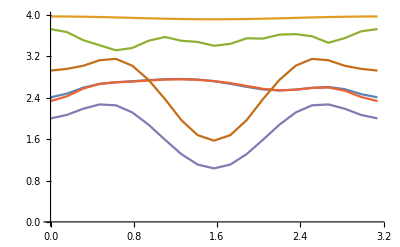

```mathematica
ListLinePlot[{rd64mean,rd64max,rd16max,rd16mean,rdmean,rdnmax}]
```

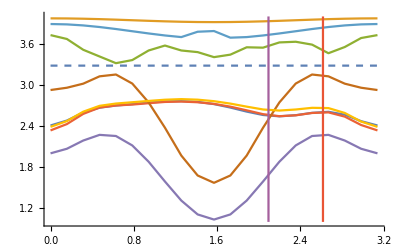

```mathematica
Show[Plot[0*x+c/.{c->3.281937853012085},{x,0,3.14},PlotStyle->Dashed],ListLinePlot[{rd64mean,rd64max,rd16max,rd16mean,rdmean,rdnmax,rd32max,rd32mean,{{2.0943951023931953,1},{2.0943951023931953,4}},,{{5Pi/6,1},{5Pi/6,4}}}],PlotRange->All]
```

#### data2

```mathematica
rd264={-0.000000000000000000*10^+00,2.000000000000000000*10^+00,3.972234460290947400*10^+00,2.226312826269990275*10^+00,6.442666605629060461*10^-01,2.171155130461605243*10^+00,3.794466733665000646*10^+00,2.395518351847664373*10^+00,1.124056318763379414*10^+00,2.357757913090019919*10^+00,3.692775718051163558*10^+00,2.669391251313184554*10^+00,1.782818610277733917*10^+00,2.368171617776035021*10^+00,3.232598640962807579*10^+00,2.425732283322516558*10^+00,1.385003977198919323*10^+00,2.479793548983265872*10^+00,3.615320906236606735*10^+00,2.581298017162434011*10^+00,1.889409568911662340*10^+00,2.487793089178919281*10^+00,3.394986106567748241*10^+00,2.801489135961738430*10^+00,2.128331065450590032*10^+00,2.196309357558596353*10^+00,2.796003156015806290*10^+00,2.681246266320277627*10^+00,1.688080722501665631*10^+00,2.287570241071511745*10^+00,3.202276978932509177*10^+00,2.661243027066238387*10^+00,1.725632663316345905*10^+00,2.069096156078668702*10^+00,2.879172054565724892*10^+00,2.724824630326948327*10^+00,2.065252721607058195*10^+00,2.039837338583355475*10^+00,2.783606436693875530*10^+00,2.416523798472264506*10^+00,1.609482597349379152*10^+00,1.958417738772101124*10^+00,2.706435106466284601*10^+00,2.309400716705633627*10^+00,1.733738228305293561*10^+00,2.268841536351517529*10^+00,2.522160301826585904*10^+00,2.570029962802766299*10^+00,2.283684783069033664*10^+00,2.139380760530615433*10^+00,2.607412189278095926*10^+00,2.653093144058281450*10^+00,1.902254731995530523*10^+00,1.769862352682032736*10^+00,2.341853720395294047*10^+00,2.729929100347536775*10^+00,2.217836569007295644*10^+00,2.039717375186066217*10^+00,2.620446609636785773*10^+00,2.593277296918016894*10^+00,2.218249941940181102*10^+00,1.836033945736257555*10^+00,2.179285921012816818*10^+00,2.415740183163995525*10^+00,2.286586436498410091*10^+00,2.165967982437650097*10^+00,2.341566998395467891*10^+00,2.424491988865511871*10^+00,2.157561433089293157*10^+00,2.035157236921590229*10^+00,2.385966341626165832*10^+00,2.691930587296310851*10^+00,2.317582241802727872*10^+00,1.928280053200105426*10^+00,2.391175961315898491*10^+00,2.885202103891516323*10^+00,2.533472918595699674*10^+00,2.143999295187600129*10^+00,2.640042358269461431*10^+00,2.831586763720912447*10^+00,2.316237390077989566*10^+00,2.030184740422715350*10^+00,2.599890016766472467*10^+00,2.570859942405236076*10^+00,2.168636439437991115*10^+00,2.158375256807544940*10^+00,2.683474351320467743*10^+00,2.799935678877269130*10^+00,2.528559328375949988*10^+00,2.564490461179963710*10^+00,2.948148806285239232*10^+00,2.905648317667024916*10^+00,2.505972514037207777*10^+00,2.494207063245787559*10^+00,2.714095232131816360*10^+00,2.679468832821764401*10^+00,2.558965818601898867*10^+00,2.600353410784550956*10^+00,2.672960029948173499*10^+00,2.460709582900062919*10^+00,2.180453659380245046*10^+00,2.453409224137162337*10^+00,2.854533270748525808*10^+00,2.615855709286149633*10^+00,2.064231715090859343*10^+00,2.230625902544737915*10^+00,2.755441620983471118*10^+00,2.469837711066652730*10^+00,1.694957090393133026*10^+00,1.992137649464228666*10^+00,2.995098020005544370*10^+00,2.530400914114466993*10^+00,1.729201564457856666*10^+00,2.204059720483436013*10^+00,2.853246457926088109*10^+00,2.559410159685370001*10^+00,2.360407361460416631*10^+00,2.449249529215552279*10^+00,2.832838841189546208*10^+00,2.577002254463636177*10^+00,2.448363149420077711*10^+00,2.306267808630272143*10^+00,2.549278733947811570*10^+00,2.380991287046221316*10^+00,2.131241013133353679*10^+00,2.148659475545970476*10^+00,2.995629637236350895*10^+00,2.798504312530762039*10^+00,2.179799019927940229*10^+00,2.238008225118348182*10^+00,2.714810570305196347*10^+00,2.721418670951559537*10^+00,2.598921292575153696*10^+00,2.477545458150181457*10^+00,2.816511806237596005*10^+00,2.945650524716445062*10^+00,2.511310736477968764*10^+00,2.084270989606460844*10^+00,2.556344808813906688*10^+00,2.614988334294030992*10^+00,2.137021152909185595*10^+00,1.716061034601291224*10^+00,2.365857956322356515*10^+00,2.579648018571996548*10^+00,2.273331362211355344*10^+00,1.833635685852365693*10^+00,2.538225124379805298*10^+00,2.665337224992207155*10^+00,1.969725873546189110*10^+00,1.883325829558295972*10^+00,2.597142259005857490*10^+00,2.559348966675353942*10^+00,1.725779058673978072*10^+00,1.822905620778093150*10^+00,2.665589041971739181*10^+00,2.669836461389689664*10^+00,1.964418145914794245*10^+00,2.064977275495508913*10^+00,2.912440873456241697*10^+00,2.666219114049419581*10^+00,1.612136827607085321*10^+00,1.713064318736760461*10^+00,2.821806298702250526*10^+00,2.760526890701602731*10^+00,1.890115538384116833*10^+00,1.988338488026855977*10^+00,2.864009330853313884*10^+00,2.974697066466894135*10^+00,2.204007374855338153*10^+00,2.298813916950609659*10^+00,3.088128300368135015*10^+00,3.320017756671451270*10^+00,2.646571372450287285*10^+00,2.432804233303107022*10^+00,3.143549684083241758*10^+00,3.193717489813012289*10^+00,2.429065281231649998*10^+00,2.392446345048260703*10^+00,3.029618388363916726*10^+00,2.715027805342164147*10^+00,1.867113965762443373*10^+00,1.997446023703076889*10^+00,2.874420629081782863*10^+00,2.654900192639523038*10^+00,1.792736361040155213*10^+00,1.538259517208707239*10^+00,2.508286376613163782*10^+00,2.708267157204056641*10^+00,2.164167092974234929*10^+00,1.887382999122367178*10^+00,2.404509217861504844*10^+00,2.982731352428527494*10^+00,1.819546866601659429*10^+00,1.644503464610457266*10^+00,2.476575804249524282*10^+00,2.945745044643184318*10^+00,2.097727640134968041*10^+00,1.367297603583751631*10^+00,2.341789817086298076*10^+00,3.343264196293304735*10^+00,2.327153279529264651*10^+00,1.454548141465380695*10^+00,2.243241347188764223*10^+00,3.194816414106885549*10^+00,2.506215270859978972*10^+00,1.542450809864134520*10^+00,2.100518395048988296*10^+00,2.920728629613015936*10^+00,2.195958186236839360*10^+00,1.622221095532501822*10^+00,2.201453590304002450*10^+00,2.976538261549305453*10^+00,2.364656797469186778*10^+00,1.439833562552364388*10^+00,2.069615762672732728*10^+00,2.961080888084636875*10^+00,2.376917801258160878*10^+00,1.845726522065102015*10^+00,2.654546312417558340*10^+00,3.337612984047295672*10^+00,2.446800403951949754*10^+00,1.689569873990915738*10^+00,2.772421820302153783*10^+00,3.448404852422337186*10^+00,2.606494020334166883*10^+00,2.162569883771318757*10^+00,3.193068000738199075*10^+00,3.731892439501893310*10^+00,2.554895641056220690*10^+00,1.857308248325836963*10^+00,2.867984023625187007*10^+00,3.456296075051160877*10^+00,2.181736006258822691*10^+00,1.295853732275182635*10^+00,2.677311004776931735*10^+00,3.418231289886219937*10^+00,1.915472689975672216*10^+00,9.320824463816735905*10^-01,2.354781330063270062*10^+00,3.528435945184476896*10^+00,2.170808344866421713*10^+00,1.533303146182009691*10^+00,2.731957449487917522*10^+00,3.525876041321836851*10^+00,2.515973579609117383*10^+00,1.997705135362166651*10^+00,2.875243911447328049*10^+00,3.433020027421965992*10^+00,2.540020533128624969*10^+00,1.984994855263733982*10^+00,2.558218084334809461*10^+00,3.256138081307590859*10^+00,2.426552577025767210*10^+00,1.761762724430487648*10^+00,2.213128279338724802*10^+00,2.912151531900869728*10^+00,2.205817596458255814*10^+00,1.723442212304038046*10^+00,2.188579780354965365*10^+00,2.820184733749213191*10^+00,2.167751921656332570*10^+00,1.848497001511848481*10^+00,2.299233797769971943*10^+00,2.960335349974634767*10^+00,2.006898004669904978*10^+00,1.796867266091125792*10^+00,2.417729891853207302*10^+00,2.936172430951041967*10^+00,1.682948779882248225*10^+00,1.811363918870704470*10^+00,2.718778144682528097*10^+00,2.537802581876750452*10^+00,1.891858187888947329*10^+00,2.048941513804092729*10^+00,2.688486649831202335*10^+00,2.578076582706425146*10^+00,1.898330337421893832*10^+00,1.904252920261529924*10^+00,2.712602911709065090*10^+00,2.889310494773131843*10^+00,1.965713996801778052*10^+00,1.812576989897096480*10^+00,2.836965219979671549*10^+00,2.624062685842532883*10^+00,1.836777702249103861*10^+00,1.704354550863236506*10^+00,2.663247639001225409*10^+00,2.917445054413621897*10^+00,1.772206058972082943*10^+00,1.858780443549146399*10^+00,3.026290255576669086*10^+00,3.172824405948715842*10^+00,2.420925543305991745*10^+00,2.440871227281125933*10^+00,3.117875877415710484*10^+00,3.047825726672954705*10^+00,2.611008168070458435*10^+00,2.777185881509878662*10^+00,3.321473234924486650*10^+00,3.219506063045859179*10^+00,2.474033663245532644*10^+00,2.452706179853084922*10^+00,3.175908050347944656*10^+00,3.294429274291067689*10^+00,2.669819115074274940*10^+00,2.711693923443768917*10^+00,3.395362929017403442*10^+00,3.134294967950812083*10^+00,2.227361113618831379*10^+00,2.420901599766724033*10^+00,3.279360427011555501*10^+00,2.735632944488968654*10^+00,1.577849263391446932*10^+00,2.188582630628863157*10^+00,3.048617521078270443*10^+00,2.759210902869074999*10^+00,1.922310967500144629*10^+00,2.338515620834968001*10^+00,2.832028092352226523*10^+00,2.269297452083987920*10^+00,1.605618434866489030*10^+00,2.329648935612309124*10^+00,2.779907353803320991*10^+00,2.286748603028736060*10^+00,1.974148341698577891*10^+00,2.438255092731401952*10^+00,2.868459821312790758*10^+00,2.607933596848456936*10^+00,2.124697199631834454*10^+00,2.323680418562351857*10^+00,2.794439680954350802*10^+00,2.661431976183481485*10^+00,2.053633311536871009*10^+00,1.980990653309993910*10^+00,2.530083838673796937*10^+00,2.348675930187533734*10^+00,2.066828916814244632*10^+00,2.461600899153312927*10^+00,2.940266686441505684*10^+00,2.686156142885684606*10^+00,2.016012884554663653*10^+00,2.320932508813487338*10^+00,2.741822178323781500*10^+00,2.858015331701358797*10^+00,1.945536314933461686*10^+00,1.963325241605709648*10^+00,2.413477380044411813*10^+00,2.533283533660604103*10^+00,2.035074402205629518*10^+00,2.273263650313258832*10^+00,2.678963905618507724*10^+00,2.852985946550983254*10^+00,2.176296117763175442*10^+00,1.995156055089738922*10^+00,2.570748430391480710*10^+00,2.846685278186645185*10^+00,2.326827623142712298*10^+00,2.151256057545028799*10^+00,2.527277895046802669*10^+00,2.439441408571027203*10^+00,2.224689505158320646*10^+00,2.523247028839321615*10^+00,2.784962204800563779*10^+00,2.546228835760766529*10^+00,2.301797550933547321*10^+00,2.517904163322514766*10^+00,2.842714307389452966*10^+00,2.810803697624628228*10^+00,2.439518392351576637*10^+00,2.558626037659614383*10^+00,2.797975135726104678*10^+00,2.644475519547429876*10^+00,2.396346407525536293*10^+00,2.408306030549690391*10^+00,2.641121546337518389*10^+00,2.686637241588382796*10^+00,2.439912712992691191*10^+00,2.130316580296578888*10^+00,2.563539158423716380*10^+00,2.765304641575329292*10^+00,2.396970229217975756*10^+00,2.124771304449067699*10^+00,2.447351879451810763*10^+00,2.681245423345951728*10^+00,2.271969423343525030*10^+00,1.878630013620119721*10^+00,2.490527534837905677*10^+00,2.863258867734289836*10^+00,2.323218370380042863*10^+00,2.177222591760424208*10^+00,2.663575928848084473*10^+00,2.845048895345112960*10^+00,2.357712788448302899*10^+00,1.911918450125311697*10^+00,2.276840015725012378*10^+00,2.949569196274859806*10^+00,2.344650907504001403*10^+00,1.513735854228799083*10^+00,2.015293183627888673*10^+00,2.964251044776632149*10^+00,2.219193746698977066*10^+00,1.440406785808703294*10^+00,2.017056031973578190*10^+00,3.119616882227231436*10^+00,2.250047262880772614*10^+00,1.456020235450897093*10^+00,1.938755518096096475*10^+00,3.023228315049554027*10^+00,2.326315901537402642*10^+00,1.796297187743937762*10^+00,2.410463642192781197*10^+00,2.845489497722701433*10^+00,2.334885056935376291*10^+00,2.383716886938101798*10^+00,2.989726408892071419*10^+00,3.029388388211316840*10^+00,2.221154307934004812*10^+00,1.992285807602751424*10^+00,2.496093375679804272*10^+00,3.102530431659301868*10^+00,2.188551224214441149*10^+00,1.957712181448515221*10^+00,2.927838780985252853*10^+00,3.106693670432500110*10^+00,1.976397380501750956*10^+00,1.632028084677220603*10^+00,2.776966697994158295*10^+00,3.454611575088669451*10^+00,2.532938899996236337*10^+00,2.026013382199144619*10^+00,2.857987596924591145*10^+00,3.062964302574232356*10^+00,2.256807978623762700*10^+00,1.946522675966587457*10^+00,2.681821670633395271*10^+00,2.848066229750836342*10^+00,2.068203628608257461*10^+00,1.988081475817010224*10^+00,2.445780737454309239*10^+00,2.538886959773088314*10^+00,2.228491266871237109*10^+00,1.952429207147322821*10^+00,2.159221904131792158*10^+00,2.508029532418279306*10^+00,2.204032756454740838*10^+00,2.418091377420428234*10^+00,2.608692518971274410*10^+00,2.458141672198452365*10^+00,2.049795700104459328*10^+00,1.882454985841738981*10^+00,2.297638431423260741*10^+00,2.449142527245366185*10^+00,2.087471099165676414*10^+00,1.853994185050447774*10^+00,2.423397532187418157*10^+00,2.893990309933341276*10^+00,2.456395768972714055*10^+00,1.968036789981030710*10^+00,2.396927314537840914*10^+00,2.501780374063494961*10^+00,2.396233538698965937*10^+00,2.307888561234487934*10^+00,2.456051943015762795*10^+00,2.026877195556789246*10^+00,1.806555163360999305*10^+00,2.038854021842423148*10^+00,2.670873047644290565*10^+00,2.071813520945246179*10^+00,1.853880085878200967*10^+00,2.344253871794365729*10^+00,2.607130825097784932*10^+00,2.026642776676368385*10^+00,1.960648880875540234*10^+00,2.520712610848934609*10^+00,3.056706286055219213*10^+00,2.470595118738981633*10^+00,2.324703002954409570*10^+00,2.593681623543545367*10^+00,3.089834191816692499*10^+00,2.825911998843949391*10^+00,2.195439534406722792*10^+00,2.465385892466795514*10^+00,3.435875744896276451*10^+00,3.322276049885915850*10^+00,2.535228771735767772*10^+00,2.525011267549707394*10^+00,3.200226992408860216*10^+00,2.947602703252403700*10^+00,2.278183619484698053*10^+00,2.304427762908963118*10^+00,3.093322659470712832*10^+00,3.023209586625434486*10^+00,1.890718430555424989*10^+00,1.834677609808545329*10^+00,2.873846852125470974*10^+00,3.159870454622034863*10^+00,2.324044937244107878*10^+00,2.238559616327759905*10^+00,3.192340468763505523*10^+00,3.194405602064936289*10^+00,2.722912528242654327*10^-14,1.999321645901668276*10^+00,3.970886869222546078*10^+00,2.475813923412640172*10^+00,9.344830299637936211*10^-01,2.435287013137991785*10^+00,3.693789305089111519*10^+00,2.388255868791109737*10^+00,1.165215524549189308*10^+00,2.354059255384929550*10^+00,3.670766065337308870*10^+00,2.859492961273256473*10^+00,2.019172443959160290*10^+00,2.578249240288247535*10^+00,3.210840215518415697*10^+00,2.443826946897438290*10^+00,1.439331982136056620*10^+00,2.531340653609590152*10^+00,3.648761823667770798*10^+00,2.774935300699292284*10^+00,2.094020531872991420*10^+00,2.580449849470668244*10^+00,3.312840577789606833*10^+00,2.806070574987975519*10^+00,2.194094852682601182*10^+00,2.275428992503994330*10^+00,2.873309059666598220*10^+00,2.863443581342318023*10^+00,1.946601979935274729*10^+00,2.483225854256280396*10^+00,3.163021433799505733*10^+00,2.702783955505499769*10^+00,1.817121826833284270*10^+00,2.082542638474656371*10^+00,2.809251678393437590*10^+00,2.783327965311864993*10^+00,2.265333809103712959*10^+00,2.187619694042828744*10^+00,2.797428549455116542*10^+00,2.459372607740784478*10^+00,1.723551202527491721*10^+00,2.030377159788325780*10^+00,2.685247644493584218*10^+00,2.382296827847818932*10^+00,1.922812634682815824*10^+00,2.417178848212833131*10^+00,2.555619985393090765*10^+00,2.586154814906444166*10^+00,2.268424287786314331*10^+00,2.154987754871803940*10^+00,2.604694732986721384*10^+00,2.725398274540793420*10^+00,2.109068037843834453*10^+00,1.932948495976483549*10^+00,2.352904277427576130*10^+00,2.712863251568288447*10^+00,2.244145319121697568*10^+00,2.105507248539324916*10^+00,2.651894531091273599*10^+00,2.739108589215311085*10^+00,2.355092736040396151*10^+00,1.940070501650454471*10^+00,2.165674667633725292*10^+00,2.472988488192972234*10^+00,2.405366212634904688*10^+00,2.319332594168723283*10^+00,2.462953699235006511*10^+00,2.551227334935822544*10^+00,2.284108199392405947*10^+00,2.095944057218791290*10^+00,2.352959651852236878*10^+00,2.705146708745335360*10^+00,2.475230041707537687*10^+00,2.107505993298546709*10^+00,2.521910750406828328*10^+00,2.932943369650512278*10^+00,2.627158101553204173*10^+00,2.208772408154788813*10^+00,2.592350841489308166*10^+00,2.769069502557672813*10^+00,2.337112066174517722*10^+00,2.129777956498825731*10^+00,2.660997192643948850*10^+00,2.686371458780399735*10^+00,2.329691386201706571*10^+00,2.309935312603168533*10^+00,2.653862314133207612*10^+00,2.755658141722919119*10^+00,2.551707588775448343*10^+00,2.677733949333616525*10^+00,3.003688088886124596*10^+00,2.955276204729555989*10^+00,2.612088580574485341*10^+00,2.534474119821830129*10^+00,2.649459163966497499*10^+00,2.680337121233359099*10^+00,2.680264228526146653*10^+00,2.765591217987508177*10^+00,2.779297263706265841*10^+00,2.570460122395409552*10^+00,2.275371402066848070*10^+00,2.492604371038241506*10^+00,2.799439506305324343*10^+00,2.645508086344640297*10^+00,2.269938283001177393*10^+00,2.408968728507461243*10^+00,2.841018187299871212*10^+00,2.619430214226240228*10^+00,1.898218993243436570*10^+00,2.104649854828635203*10^+00,2.905950411460735516*10^+00,2.540221880768182672*10^+00,1.890231972121941606*10^+00,2.300221504372193415*10^+00,2.882009681758514574*10^+00,2.648969551069452422*10^+00,2.487101606977861312*10^+00,2.560277211985916068*10^+00,2.844270789277630662*10^+00,2.597959706572951610*10^+00,2.510726671555322476*10^+00,2.403705255781625638*10^+00,2.584685059149824049*10^+00,2.472421752071943590*10^+00,2.307872500130018434*10^+00,2.313137130005664233*10^+00,3.002049653409706309*10^+00,2.778260415585700027*10^+00,2.161789706270725198*10^+00,2.262728162276903987*10^+00,2.704530439848533252*10^+00,2.775766852066623436*10^+00,2.731560523089611614*10^+00,2.632287826310367951*10^+00,2.895341194320749434*10^+00,2.950329493485472909*10^+00,2.546884444431136263*10^+00,2.110085870877450809*10^+00,2.488221874954996249*10^+00,2.652368141032424020*10^+00,2.281032686011582378*10^+00,1.930767456418508443*10^+00,2.448533600555701462*10^+00,2.579934885088409402*10^+00,2.345032827027812239*10^+00,1.932219758095135465*10^+00,2.572709267305793635*10^+00,2.649489043429060331*10^+00,2.105960432165788099*10^+00,2.054417534031488302*10^+00,2.620071669914542323*10^+00,2.558744029394822928*10^+00,1.809584549284140920*10^+00,1.868045744140855557*10^+00,2.627289783881584739*10^+00,2.696017584557202973*10^+00,2.118582281818650603*10^+00,2.255228048894390103*10^+00,2.986542496983122241*10^+00,2.684704511633650093*10^+00,1.732042834838697587*10^+00,1.798717108671313625*10^+00,2.770586344992489458*10^+00,2.811290126288679581*10^+00,2.096415794700882351*10^+00,2.218108002236233833*10^+00,2.998461579682804246*10^+00,2.985605720277391573*10^+00,2.306578077943549410*10^+00,2.357266128816905670*10^+00,3.067821628778206744*10^+00,3.327677068808796879*10^+00,2.796226554859481350*10^+00,2.623621417301812198*10^+00,3.192703877876135188*10^+00,3.176193206819928783*10^+00,2.503822053877065024*10^+00,2.459002665961413037*10^+00,3.010671145878488719*10^+00,2.756887711709802957*10^+00,2.078049273200067937*10^+00,2.188696274650731244*10^+00,2.914162409478100901*10^+00,2.635522269250096361*10^+00,1.836128513711632326*10^+00,1.597187889815148365*10^+00,2.499202948134540581*10^+00,2.681114943060908473*10^+00,2.237579520562586133*10^+00,2.017920366730578507*10^+00,2.484364626416971866*10^+00,2.962944629806700814*10^+00,1.942767892364864135*10^+00,1.778997989131618551*10^+00,2.520843448418749411*10^+00,2.906190903913911772*10^+00,2.227582985138246929*10^+00,1.571358114403054840*10^+00,2.436316522540784124*10^+00,3.342460446216412251*10^+00,2.443408063764296312*10^+00,1.673269587241352774*10^+00,2.345720615838418510*10^+00,3.181723730570121589*10^+00,2.660556349838937074*10^+00,1.754353948159150356*10^+00,2.221253005930015512*10^+00,2.880475299166195047*10^+00,2.253067872254379544*10^+00,1.736450810428442182*10^+00,2.236153809650388347*10^+00,3.027545671744975575*10^+00,2.513989552759225088*10^+00,1.715977781211631470*10^+00,2.212321234919956137*10^+00,2.962360710559941435*10^+00,2.448853896046231160*10^+00,1.987656648916815483*10^+00,2.675040892332487097*10^+00,3.297877495050443919*10^+00,2.560825081168012662*10^+00,1.867168418757544801*10^+00,2.865917296783966339*10^+00,3.469920699296603850*10^+00,2.734935966517857864*10^+00,2.331566658511690537*10^+00,3.205630978293467770*10^+00,3.638911032836706472*10^+00,2.681953664936422399*10^+00,2.114904747907351279*10^+00,3.004291236684880406*10^+00,3.436753557178521046*10^+00,2.351619952527281399*10^+00,1.534256162201627749*10^+00,2.752663630430230324*10^+00,3.361441349261578893*10^+00,2.088787059433115711*10^+00,1.212014897768134647*10^+00,2.496481255159618939*10^+00,3.503657113442471438*10^+00,2.212647028016108131*10^+00,1.652710498943492645*10^+00,2.754727537603607779*10^+00,3.454181584135382455*10^+00,2.613861893626530541*10^+00,2.168870845594367935*10^+00,2.972499987213498507*10^+00,3.406778743931906828*10^+00,2.599255057082836551*10^+00,2.162267579442262999*10^+00,2.666607044247803593*10^+00,3.262032571337809550*10^+00,2.622098712007922661*10^+00,2.020241272443148439*10^+00,2.393756488850665498*10^+00,2.880144691852922101*10^+00,2.238599747959003405*10^+00,1.862087136334788173*10^+00,2.310644189618339173*10^+00,2.838969832438603902*10^+00,2.335634047583371675*10^+00,2.064052878946898595*10^+00,2.488234076203907463*10^+00,2.912817828687570110*10^+00,2.037011064250802583*10^+00,1.904711751249920093*10^+00,2.560427498411725011*10^+00,3.034687475285740010*10^+00,1.913616380213063684*10^+00,2.078182347750947123*10^+00,2.909760121414382006*10^+00,2.628289277283636594*10^+00,1.998536181897646591*10^+00,2.152272531667717370*10^+00,2.719101542326817889*10^+00,2.637617612098400066*10^+00,2.070652501932579437*10^+00,2.093784173995403286*10^+00,2.839809958677206758*10^+00,2.914789865026830462*10^+00,2.075505506904759656*10^+00,2.019491561222999998*10^+00,2.929858549883665120*10^+00,2.752186489961106375*10^+00,2.043176792689133325*10^+00,1.952414992161366269*10^+00,2.838704863146973345*10^+00,2.934081532622395017*10^+00,1.855239400286495810*10^+00,2.001966823816823560*10^+00,3.081793561270822046*10^+00,3.231189393873729720*10^+00,2.603802305753434077*10^+00,2.675510919721073133*10^+00,3.210875667153623603*10^+00,3.079491309145567790*10^+00,2.679738004498347870*10^+00,2.814813666489974775*10^+00,3.278166772702660658*10^+00,3.198709295604020397*10^+00,2.571767289814942181*10^+00,2.576737279574263795*10^+00,3.181936543843819631*10^+00,3.278606917185463043*10^+00,2.719247702057988825*10^+00,2.775852483055087916*10^+00,3.417796104922423250*10^+00,3.193271644891120697*10^+00,2.428987195634272567*10^+00,2.615903112129428720*10^+00,3.319373938464854845*10^+00,2.766356667842831740*10^+00,1.686483491178149663*10^+00,2.297021012678017282*10^+00,3.056317959447826915*10^+00,2.799647568268277098*10^+00,2.125838911939677889*10^+00,2.507371094897982822*10^+00,2.858094263684139769*10^+00,2.281334318615495960*10^+00,1.659471735962857908*10^+00,2.362767180497254760*10^+00,2.806075113720312597*10^+00,2.375307847713842957*10^+00,2.167429761867111004*10^+00,2.627432494186078049*10^+00,2.920432274639088277*10^+00,2.582209787025274039*10^+00,2.164507570930711999*10^+00,2.417642385412666517*10^+00,2.822921507067162494*10^+00,2.739069605164138110*10^+00,2.252923695588625375*10^+00,2.210522918270658721*10^+00,2.604589112943787477*10^+00,2.322838815516159894*10^+00,2.056279568984111350*10^+00,2.495773288186523331*10^+00,2.974116351705331063*10^+00,2.830763723912736562*10^+00,2.234045429250308246*10^+00,2.559178866752131576*10^+00,2.859947779768985843*10^+00,2.853402573103715589*10^+00,2.000590877328599859*10^+00,2.015173591763347094*10^+00,2.455306678942839049*10^+00,2.631272942098390466*10^+00,2.208292818618645459*10^+00,2.477862015862287048*10^+00,2.763000689956626399*10^+00,2.808569354980178456*10^+00,2.231590216039111230*10^+00,2.124285658247996089*10^+00,2.665276919465456196*10^+00,2.948256603195406278*10^+00,2.462550327631357838*10^+00,2.269052138839893651*10^+00,2.568613933903347579*10^+00,2.423396216739361897*10^+00,2.297111952879351549*10^+00,2.580026573430139969*10^+00,2.785443476747819780*10^+00,2.588512506123948675*10^+00,2.407966245319834275*10^+00,2.643411137106201458*10^+00,2.933873466008279696*10^+00,2.833994227290549617*10^+00,2.520201368537956288*10^+00,2.678554697066441115*10^+00,2.841846745995108225*10^+00,2.745248967676098495*10^+00,2.507097664853487728*10^+00,2.508206489594282385*10^+00,2.714278295692960530*10^+00,2.760873071060177875*10^+00,2.555765780539775989*10^+00,2.288991345849798353*10^+00,2.645008950364263089*10^+00,2.808235965781763266*10^+00,2.503264666659447801*10^+00,2.248558493817901294*10^+00,2.563480280244510912*10^+00,2.791845268388255530*10^+00,2.424308477044518462*10^+00,2.059978871035053949*10^+00,2.532438003018457895*10^+00,2.786082978838081203*10^+00,2.386864941920373795*10^+00,2.299160137609262300*10^+00,2.715501544414716140*10^+00,2.889697716376649517*10^+00,2.513678530265741617*10^+00,2.157517098635647113*10^+00,2.395549461264212088*10^+00,2.876103157784066333*10^+00,2.413549842607542573*10^+00,1.649840351564493712*10^+00,2.054225139171045100*10^+00,2.939776153442961615*10^+00,2.299742590601430603*10^+00,1.650461895377328236*10^+00,2.153592352212088112*10^+00,3.007475829031280412*10^+00,2.250989370680389179*10^+00,1.575482940004878873*10^+00,2.026343688456844649*10^+00,2.978733457603446766*10^+00,2.408349953826598888*10^+00,1.952038414002537081*10^+00,2.556266768505292664*10^+00,2.807124040905320861*10^+00,2.384421703382730406*10^+00,2.450834711580302638*10^+00,2.953777340645783234*10^+00,3.029900053330010667*10^+00,2.327505835489660502*10^+00,2.210127979888465433*10^+00,2.685491047216523874*10^+00,3.091950072304546548*10^+00,2.251631200973145841*10^+00,2.082510935444541911*10^+00,2.930924175145112720*10^+00,3.066822037920713839*10^+00,2.047973864034262181*10^+00,1.761346543522432251*10^+00,2.868992693044177589*10^+00,3.419679053028546800*10^+00,2.660711834115133456*10^+00,2.249589586004118846*10^+00,2.902726410302630455*10^+00,3.050752916429571471*10^+00,2.341894585830535114*10^+00,2.137343493444470610*10^+00,2.854389328060183750*10^+00,2.869958867301985350*10^+00,2.131413059497702100*10^+00,2.043639954188654073*10^+00,2.428330983460382786*10^+00,2.524210802023099998*10^+00,2.304308815516540765*10^+00,2.094449528348175882*10^+00,2.309399626328963340*10^+00,2.546221312971320927*10^+00,2.255906465296793506*10^+00,2.503832698328774420*10^+00,2.646484532379160370*10^+00,2.494230981093373600*10^+00,2.126542853943488076*10^+00,1.978064636451423830*10^+00,2.349366483394357275*10^+00,2.395271266843374214*10^+00,2.072367487388668827*10^+00,1.849804559223088729*10^+00,2.381547041128697195*10^+00,2.818478343041671774*10^+00,2.520573307479602843*10^+00,2.136109100932912952*10^+00,2.500605204355102362*10^+00,2.522167917619710487*10^+00,2.385796141417620309*10^+00,2.303456691622788988*10^+00,2.438308108064693336*10^+00,2.109347467788645236*10^+00,1.906611335181400690*10^+00,2.173437255369524035*10^+00,2.679365971715925721*10^+00,2.043658202624941467*10^+00,1.930692162352492414*10^+00,2.503121622462016305*10^+00,2.713936783366524885*10^+00,2.210102707276414780*10^+00,2.134535840423256392*10^+00,2.672347956666792701*10^+00,3.100536841271297472*10^+00,2.443409233173402306*10^+00,2.305358918784453426*10^+00,2.542621920330591312*10^+00,3.018712375451121588*10^+00,2.812149368482814715*10^+00,2.344847917623404498*10^+00,2.665637178840547072*10^+00,3.478472806829250530*10^+00,3.332218372514082816*10^+00,2.594540800587752383*10^+00,2.571350275893764525*10^+00,3.157761631937710423*10^+00,2.941617453335898968*10^+00,2.417525573799069960*10^+00,2.483104962848878827*10^+00,3.140650005203278639*10^+00,3.056436357433858664*10^+00,2.076511148523515260*10^+00,2.000336172844533245*10^+00,2.869472469917400126*10^+00,3.126388461994261903*10^+00,2.366678457824581638*10^+00,2.327183676542553314*10^+00,3.206873279739467897*10^+00,3.215703723804872460*10^+00,-9.610279511444755881*10^-16,1.997353286798289496*10^+00,3.966980812630833686*10^+00,2.827593514006927489*10^+00,1.413558390924810837*10^+00,2.763908212783971585*10^+00,3.471025900019582000*10^+00,2.375087994812096870*10^+00,1.268884273348221958*10^+00,2.359319063320244325*10^+00,3.616671039003560573*10^+00,3.129047955229703692*10^+00,2.329138240331777965*10^+00,2.851604748852630156*10^+00,3.114671195997258835*10^+00,2.458622913603218940*10^+00,1.579300560090456385*10^+00,2.616980127686232560*10^+00,3.679066694954892025*10^+00,3.042497646073661244*10^+00,2.429191580681450802*10^+00,2.637587644494596262*10^+00,3.085809562683992979*10^+00,2.774811879260579595*10^+00,2.341162593853835627*10^+00,2.390272464644837225*10^+00,2.928615573899068458*10^+00,3.096488361860699090*10^+00,2.325804690647584660*10^+00,2.711983811262845379*10^+00,3.079638933041383808*10^+00,2.748257390831176483*10^+00,2.011013564301256551*10^+00,2.123437785228774022*10^+00,2.664724432247571162*10^+00,2.903592183029416685*10^+00,2.536836908636349808*10^+00,2.417189361070908316*10^+00,2.858438259073876608*10^+00,2.529837100194358257*10^+00,1.987147465282279590*10^+00,2.181961884717991573*10^+00,2.630395887135898114*10^+00,2.544504355884257940*10^+00,2.223392783532505135*10^+00,2.650129526446678874*10^+00,2.684953322608522264*10^+00,2.626056378674352487*10^+00,2.259586219901272841*10^+00,2.179120002958065072*10^+00,2.587094820242096915*10^+00,2.844357637945363670*10^+00,2.401047051717246639*10^+00,2.254900761590741265*10^+00,2.377591011348624939*10^+00,2.665471251211299908*10^+00,2.312759274093897144*10^+00,2.236377181765371702*10^+00,2.709648429431979366*10^+00,2.954450777065338762*10^+00,2.613864642858118259*10^+00,2.117926125848184959*10^+00,2.139470211911187469*10^+00,2.600394303112830041*10^+00,2.651350838293034418*10^+00,2.538758704510421627*10^+00,2.644858393296872112*10^+00,2.800642397012212736*10^+00,2.515597922174841905*10^+00,2.164087586701660015*10^+00,2.266662716657606325*10^+00,2.743938495321685878*10^+00,2.778961622546089139*10^+00,2.386245278971873329*10^+00,2.696305162878412709*10^+00,3.081998156357871554*10^+00,2.779889157874690042*10^+00,2.287995718814365365*10^+00,2.461319554391275588*10^+00,2.664683166948172754*10^+00,2.399344756514973476*10^+00,2.295740751605333418*10^+00,2.777695300729282391*10^+00,2.884495898702308825*10^+00,2.550989369327224754*10^+00,2.494145219113713896*10^+00,2.573348581877933139*10^+00,2.665263031090039370*10^+00,2.631511429916499445*10^+00,2.841293152581832349*10^+00,3.124262375592348207*10^+00,3.099409158367478323*10^+00,2.797822234347355774*10^+00,2.592239709172612372*10^+00,2.527084367259798015*10^+00,2.716197876231216224*10^+00,2.930995822590603428*10^+00,2.954841162315756442*10^+00,2.874842029126205567*10^+00,2.835873265004523081*10^+00,2.481645508772873931*10^+00,2.514277599666828067*10^+00,2.672808162337243054*10^+00,2.725094680860769447*10^+00,2.703185640531032607*10^+00,2.643723716328484130*10^+00,2.922991755097361199*10^+00,2.903342056237754321*10^+00,2.252467403633696019*10^+00,2.214279971783874146*10^+00,2.680176803845585543*10^+00,2.525840187122276426*10^+00,2.200099411756869738*10^+00,2.468105501181771633*10^+00,2.925227646205691201*10^+00,2.855677346673481942*10^+00,2.731637643896664969*10^+00,2.710526109137686213*10^+00,2.815297296951447148*10^+00,2.608371411669734741*10^+00,2.643471112468417150*10^+00,2.564204632722954180*10^+00,2.616154019032096656*10^+00,2.598460116115989482*10^+00,2.620035420121864966*10^+00,2.608287509828785655*10^+00,2.995833808494027473*10^+00,2.668773656214801449*10^+00,2.103576140651671977*10^+00,2.310457242482090834*10^+00,2.665936930136792782*10^+00,2.780551422974851583*10^+00,2.949469332338627403*10^+00,2.884498524295262101*10^+00,2.975452811506786421*10^+00,2.886593136992182451*10^+00,2.621266087979111870*10^+00,2.167412034367236728*10^+00,2.323083725866543325*10^+00,2.689983666379654803*10^+00,2.595635932081472141*10^+00,2.340551073729312037*10^+00,2.564565751761063606*10^+00,2.572842886267798779*10^+00,2.470259021367322116*10^+00,2.134225197593543122*10^+00,2.588875021739570848*10^+00,2.635535618285295811*10^+00,2.329336282570038552*10^+00,2.356306965911683982*10^+00,2.651474430567941187*10^+00,2.523192790793939100*10^+00,2.003451953442158207*10^+00,1.944690408155031802*10^+00,2.533934072652733072*10^+00,2.730261129212707694*10^+00,2.468391056967514263*10^+00,2.549945236346472743*10^+00,3.047304921414673906*10^+00,2.701058274247810864*10^+00,2.026677904649102580*10^+00,1.950515209948248785*10^+00,2.609444660683274186*10^+00,2.855615836401737884*10^+00,2.498521137416125359*10^+00,2.558614508772186991*10^+00,3.092886530313642357*10^+00,3.001887150651920688*10^+00,2.558697204282804893*10^+00,2.501430652671268628*10^+00,2.999701219050523893*10^+00,3.327806661713519354*10^+00,3.072803767599634917*10^+00,2.924391571464641348*10^+00,3.296505332906001673*10^+00,3.147307366294664455*10^+00,2.648130337491662711*10^+00,2.636937925854161868*10^+00,2.952035303780727205*10^+00,2.834486684384868393*10^+00,2.472254049204550164*10^+00,2.520746819665832916*10^+00,2.957633179530968270*10^+00,2.582399759145372897*10^+00,1.978370251151582160*10^+00,1.753835393826741917*10^+00,2.463127680578230283*10^+00,2.599450224626524086*10^+00,2.360032320918309168*10^+00,2.301136395655967171*10^+00,2.618020688816949715*10^+00,2.924379640752208687*10^+00,2.150725562405282343*10^+00,2.054758202290561719*10^+00,2.589226592259484594*10^+00,2.831107021380784960*10^+00,2.454244250759634483*10^+00,1.940293186774961542*10^+00,2.572110527684964509*10^+00,3.324092937078130916*10^+00,2.658005394110372510*10^+00,2.033319485480746813*10^+00,2.492869317177792254*10^+00,3.155935404935370059*10^+00,2.947621691602015925*10^+00,2.141489069515448929*10^+00,2.384682760037446059*10^+00,2.785282445690477893*10^+00,2.351383701284212258*10^+00,1.979439823862157111*10^+00,2.292755428871843471*10^+00,3.059369907304689384*10^+00,2.804267187981856591*10^+00,2.238867647306734820*10^+00,2.433335315173381641*10^+00,2.907571617168500211*10^+00,2.543672363514994039*10^+00,2.263960773689509320*10^+00,2.709076243863900668*10^+00,3.220785547964618800*10^+00,2.779482813631756866*10^+00,2.222006031803760884*10^+00,2.987146118385687110*10^+00,3.493642700881136154*10^+00,2.978968579083944412*10^+00,2.666042158584671640*10^+00,3.266980603650265547*10^+00,3.435731399610351566*10^+00,2.933210680871899623*10^+00,2.578302841622217567*10^+00,3.197333316722908769*10^+00,3.412666831673281109*10^+00,2.635928393751078680*10^+00,1.971223898423358545*10^+00,2.889546819353760121*10^+00,3.249428413987478947*10^+00,2.344750587232069972*10^+00,1.743465112343245860*10^+00,2.743375067331633943*10^+00,3.427277196703092610*10^+00,2.350890193855087684*10^+00,1.923675465347672642*10^+00,2.805265358292932998*10^+00,3.302674375362866233*10^+00,2.787416867566727241*10^+00,2.492859122473428002*10^+00,3.132761837309035347*10^+00,3.344380211845953355*10^+00,2.748596075676178696*10^+00,2.501664594403246955*10^+00,2.921324970498682116*10^+00,3.274944590943050571*10^+00,2.907594585783934704*10^+00,2.434211039684852196*10^+00,2.718904392545122839*10^+00,2.814247396209686336*10^+00,2.321669128641332236*10^+00,2.168989769960387726*10^+00,2.555135991819730279*10^+00,2.841398321848362052*10^+00,2.569465884825634205*10^+00,2.429901450744850422*10^+00,2.827461966065082155*10^+00,2.835113971101847596*10^+00,2.088369376101661512*10^+00,2.148677761530042751*10^+00,2.824191110094163015*10^+00,3.154149481737112737*10^+00,2.233523065538439045*10^+00,2.493682575181393801*10^+00,3.180981476811721720*10^+00,2.745958704899901459*10^+00,2.229991446151275980*10^+00,2.361065985263600009*10^+00,2.763847799137854722*10^+00,2.718812863665581947*10^+00,2.392385000147901675*10^+00,2.442827203456776175*10^+00,3.008222083049782114*10^+00,2.909729562903689448*10^+00,2.220620892182176398*10^+00,2.371350647931630640*10^+00,3.101866182631195290*10^+00,2.891085580577487768*10^+00,2.331596353237926245*10^+00,2.377083952830657765*10^+00,3.117872499721795698*10^+00,2.960681859086595313*10^+00,1.970917755978954133*10^+00,2.279752932755634731*10^+00,3.177422078752196288*10^+00,3.306784084239903887*10^+00,2.850871738839842795*10^+00,3.020764234115071556*10^+00,3.373579705919033778*10^+00,3.135827306811071136*10^+00,2.806004011224805694*10^+00,2.883181889032548462*10^+00,3.179491130622124739*10^+00,3.141028433206182413*10^+00,2.737062793815038475*10^+00,2.764577136057476903*10^+00,3.135979941295676809*10^+00,3.186188899957387299*10^+00,2.787957213998239148*10^+00,2.922320240688766280*10^+00,3.446071388612657493*10^+00,3.262192088576181703*10^+00,2.711217957365618769*10^+00,2.937823542283179101*10^+00,3.376462896966016647*10^+00,2.755774776687317740*10^+00,1.880072071792286970*10^+00,2.493112290306691126*10^+00,3.098454564717084914*10^+00,2.864360524018968235*10^+00,2.500316102511425775*10^+00,2.812654720499804917*10^+00,2.834881050627220400*10^+00,2.224401957053928847*10^+00,1.765688099421331758*10^+00,2.476684036682516687*10^+00,2.869304147412339301*10^+00,2.491129751826410388*10^+00,2.437070942001512641*10^+00,2.940526404487783019*10^+00,2.962285832491533544*10^+00,2.481709445657195978*10^+00,2.225646346501763073*10^+00,2.649842483613327637*10^+00,2.920127099451687247*10^+00,2.877689163896417934*10^+00,2.599397760140920166*10^+00,2.600805861576689360*10^+00,2.735142799041859973*10^+00,2.264023778763924355*10^+00,2.036298060472035321*10^+00,2.623576510125688710*10^+00,3.078035927501297842*10^+00,3.041024136262354016*10^+00,2.527705785740043787*10^+00,2.886936358484661902*10^+00,3.057090280976588748*10^+00,2.821855440189754649*10^+00,2.133343084504602860*10^+00,2.177603969703424625*10^+00,2.578745028770873748*10^+00,2.793786303096859491*10^+00,2.512753851982428621*10^+00,2.812229039000108344*10^+00,2.870334714822475597*10^+00,2.676233189941294999*10^+00,2.303945330457778162*10^+00,2.355788661882273871*10^+00,2.821511849220714740*10^+00,3.131925054104427453*10^+00,2.736688563615433001*10^+00,2.502937887639570036*10^+00,2.585202176835260435*10^+00,2.357454443724423143*10^+00,2.385747779028857263*10^+00,2.703832224278902352*10^+00,2.810747375382726787*10^+00,2.676056128022323843*10^+00,2.630149553849217448*10^+00,2.838966211154089869*10^+00,3.050096570095809589*10^+00,2.883584360699660287*10^+00,2.707675688638556011*10^+00,2.911468221361662945*10^+00,2.963573062611191578*10^+00,2.936340883424191972*10^+00,2.725218055746735590*10^+00,2.660367256213267417*10^+00,2.812004702775726450*10^+00,2.863734970993679241*10^+00,2.703591895393703481*10^+00,2.499247677124347256*10^+00,2.802022893524494851*10^+00,2.941597000018683961*10^+00,2.689509967890656661*10^+00,2.461518801201348694*10^+00,2.756557266283308216*10^+00,2.920949276407399875*10^+00,2.689193064530742916*10^+00,2.459897079379167018*10^+00,2.621027003269619460*10^+00,2.633688507051403782*10^+00,2.477594144081626037*10^+00,2.566650336364320051*10^+00,2.831677326552108021*10^+00,2.991889475072313065*10^+00,2.834256954689830632*10^+00,2.613061110218041883*10^+00,2.620480326427904849*10^+00,2.710286628956761312*10^+00,2.509717181141233766*10^+00,1.942527736492799750*10^+00,2.161084944904734684*10^+00,2.852743650270591402*10^+00,2.468433534573549970*10^+00,2.070885456684976589*10^+00,2.359625617247597340*10^+00,2.757390380153070364*10^+00,2.224601017451052876*10^+00,1.811621650298000930*10^+00,2.199189651703993942*10^+00,2.920347106338078813*10^+00,2.555081512178498659*10^+00,2.285291181201408950*10^+00,2.791418483635021985*10^+00,2.766641941591056586*10^+00,2.471760231364764859*10^+00,2.583728785667038341*10^+00,2.882362611448944012*10^+00,3.043685407281059518*10^+00,2.622255903093914320*10^+00,2.581339822979740184*10^+00,2.970192904862901884*10^+00,3.106796218790593311*10^+00,2.341973148722136688*10^+00,2.297829039083093328*10^+00,2.925118508548785634*10^+00,2.977851768354126794*10^+00,2.232415086667315585*10^+00,1.979079886813148059*10^+00,2.995094407487862931*10^+00,3.316450886680604171*10^+00,2.823893187778860003*10^+00,2.646323376939639704*10^+00,2.983532785398713916*10^+00,3.050059868895074189*10^+00,2.500416537252929672*10^+00,2.466174998527142392*10^+00,3.101928456739923678*10^+00,2.944216187008767527*10^+00,2.234679757410382717*10^+00,2.154763662781355116*10^+00,2.409583445190928597*10^+00,2.542495103680883162*10^+00,2.455302643460739009*10^+00,2.363037416999569373*10^+00,2.570826471917995626*10^+00,2.591913727873934814*10^+00,2.331547994717088734*10^+00,2.642527467364349292*10^+00,2.736304268936868844*10^+00,2.520783483577597295*10^+00,2.275300378214225816*10^+00,2.199818442852958356*10^+00,2.483463308586489227*10^+00,2.306809997966398740*10^+00,2.043669163693183410*10^+00,1.863247127456636898*10^+00,2.260151396873979035*10^+00,2.658550704030903766*10^+00,2.670812884531529985*10^+00,2.414416695167022731*10^+00,2.641954344274285660*10^+00,2.568553941951116304*10^+00,2.396282806408658761*10^+00,2.272417716284046652*10^+00,2.413100354392787583*10^+00,2.251139836040379372*10^+00,2.121289837389501276*10^+00,2.412188519203761317*10^+00,2.681648761367443345*10^+00,2.027420091882758069*10^+00,2.103459876551551311*10^+00,2.770141619253106313*10^+00,2.889217498782009841*10^+00,2.483696283435860686*10^+00,2.414111390232452692*10^+00,2.926124612887289533*10^+00,3.160059595450007919*10^+00,2.440587707122752636*10^+00,2.275460720514331570*10^+00,2.452142475862540749*10^+00,2.848233806629486775*10^+00,2.833002990981499103*10^+00,2.601428861351321675*10^+00,2.909678173325154216*10^+00,3.539702638031659632*10^+00,3.334886164821005750*10^+00,2.708582407554481986*10^+00,2.627658434017905442*10^+00,3.038545388005533532*10^+00,2.948314102398475800*10^+00,2.697438916066712267*10^+00,2.740104613893326491*10^+00,3.219248134446993426*10^+00,3.121305380793953699*10^+00,2.400583904088483767*10^+00,2.292072395102781712*10^+00,2.827806350144626002*10^+00,3.056554005532107876*10^+00,2.488832652956995517*10^+00,2.527368385230408521*10^+00,3.223522822384237596*10^+00,3.232607125579336493*10^+00,9.610279511444749964*10^-16,1.994288388562598824*10^+00,3.960908447015873524*10^+00,2.993811126825866697*10^+00,1.791934672090820246*10^+00,3.015639899506587174*10^+00,3.267006071134518574*10^+00,2.311561399011027973*10^+00,1.407599558615552748*10^+00,2.412457426759614165*10^+00,3.567916228322573602*10^+00,3.233364890344033071*10^+00,2.521203300135527847*10^+00,2.977925457335054205*10^+00,2.966909204292361935*10^+00,2.439803849032528227*10^+00,1.715450782241968231*10^+00,2.668861973378966468*10^+00,3.649787335733853055*10^+00,3.213231397229758812*10^+00,2.645379352897241798*10^+00,2.578288652295488426*10^+00,2.800347937361736150*10^+00,2.780614960643944755*10^+00,2.472811834670797015*10^+00,2.448951385127084102*10^+00,2.905239367791997651*10^+00,3.189267601911351946*10^+00,2.584873285410642652*10^+00,2.833739622607179154*10^+00,2.987543368015043388*10^+00,2.729552916703031240*10^+00,2.199216208720813359*10^+00,2.185748412656033590*10^+00,2.524188099456408541*10^+00,2.944131716219245298*10^+00,2.696879226704936627*10^+00,2.627256987322292847*10^+00,2.868548962840260064*10^+00,2.553449508804636725*10^+00,2.241818080946195835*10^+00,2.363774534152798701*10^+00,2.600858513331115507*10^+00,2.687790940774447801*10^+00,2.454370227527277848*10^+00,2.884351692813839740*10^+00,2.887709226321170775*10^+00,2.686268143623012694*10^+00,2.251639737375461969*10^+00,2.225587999333576761*10^+00,2.595114940897384148*10^+00,2.921116988825913641*10^+00,2.619491574671396705*10^+00,2.533776903498106137*10^+00,2.468466555196072942*10^+00,2.652758798485588265*10^+00,2.405101628960358617*10^+00,2.337434793448653902*10^+00,2.734865626590287757*10^+00,3.099050086891376843*10^+00,2.775530185199674538*10^+00,2.256144122673680918*10^+00,2.207468785851668613*10^+00,2.757556860491275685*10^+00,2.845772531756517232*10^+00,2.678940965219196890*10^+00,2.821067380808509828*10^+00,3.006534988150439514*10^+00,2.663740480472777783*10^+00,2.160012393603665259*10^+00,2.211975419620725969*10^+00,2.796770020613219110*10^+00,2.997892179375036825*10^+00,2.553687501434797280*10^+00,2.797862232658656634*10^+00,3.204078126641960900*10^+00,2.831208564573234554*10^+00,2.271332410209922159*10^+00,2.345094196468612502*10^+00,2.626809703727501333*10^+00,2.489001970527923380*10^+00,2.429924689833083740*10^+00,2.859877740132636958*10^+00,2.980702483624169119*10^+00,2.660394962152981879*10^+00,2.540082726665590762*10^+00,2.511689895503084635*10^+00,2.646897418376243483*10^+00,2.733772969371394801*10^+00,2.932610016673975917*10^+00,3.173642685256561791*10^+00,3.235034344919267113*10^+00,2.918495918024140767*10^+00,2.555580146330809654*10^+00,2.421740271592397242*10^+00,2.802318623729198155*10^+00,3.117367108158123568*10^+00,2.996940157214260214*10^+00,2.918281765179167042*10^+00,3.058709126030852765*10^+00,2.682201997992554432*10^+00,2.472248014951020867*10^+00,2.509247125672773304*10^+00,2.837799218596214423*10^+00,3.049785043587441180*10^+00,2.721937268396382947*10^+00,2.887851850548034172*10^+00,3.146297323617814445*10^+00,2.542203669476301719*10^+00,2.173656772353699917*10^+00,2.327056048798534782*10^+00,2.495184044692258851*10^+00,2.485062869861199619*10^+00,2.542818344278026998*10^+00,2.897570431976193017*10^+00,3.053003217892791721*10^+00,2.954491490936495879*10^+00,2.758723085681465736*10^+00,2.684590331140369823*10^+00,2.625408192168440458*10^+00,2.754759338498108612*10^+00,2.630376760018199533*10^+00,2.579661776026293207*10^+00,2.657470197952763069*10^+00,2.848466699628797727*10^+00,2.798522162174766237*10^+00,2.879353500165002799*10^+00,2.478054941686957946*10^+00,2.043984434830221630*10^+00,2.361719065784601668*10^+00,2.649256741451903263*10^+00,2.724978352089715283*10^+00,3.099608165864327081*10^+00,3.060652375991667284*10^+00,2.918782267921465667*10^+00,2.801077168723622002*10^+00,2.706203952085874942*10^+00,2.221926744739494808*10^+00,2.152972500988854065*10^+00,2.638974043333059516*10^+00,2.866340526730423388*10^+00,2.646978022689276067*10^+00,2.614041760615705812*10^+00,2.572015748081388331*10^+00,2.601557981688431109*10^+00,2.295705530077691403*10^+00,2.559776934047395258*10^+00,2.555435158471250467*10^+00,2.412964568719041303*10^+00,2.513803714712199877*10^+00,2.601468311082976825*10^+00,2.559184391798826841*10^+00,2.217281547760298288*10^+00,2.003856056851368805*10^+00,2.405462609481400449*10^+00,2.743146428845548712*10^+00,2.782982672544918490*10^+00,2.718990643810977659*10^+00,2.940183496497195570*10^+00,2.749923319908546659*10^+00,2.347259449593531944*10^+00,2.101392159319245945*10^+00,2.380100525481623208*10^+00,2.843489610450096183*10^+00,2.814154896399160055*10^+00,2.762054227494975756*10^+00,3.018933271346288638*10^+00,3.012538682642180277*10^+00,2.875833191527770616*10^+00,2.664647630048472937*10^+00,2.886376832293126693*10^+00,3.275014430033132307*10^+00,3.229190918430139945*10^+00,3.103367703155126112*10^+00,3.292870185697007290*10^+00,3.086606884781113891*10^+00,2.780166221920479686*10^+00,2.763108205543844065*10^+00,2.814047865747525634*10^+00,2.838422374927893177*10^+00,2.796408817936206770*10^+00,2.731558081306092234*10^+00,2.931149057524320867*10^+00,2.573123646408579823*10^+00,2.164680994242636380*10^+00,1.924809096181250956*10^+00,2.416111282703612861*10^+00,2.477962236183795852*10^+00,2.396172472046727897*10^+00,2.451437004996909419*10^+00,2.663966021357871750*10^+00,2.843876742075994724*10^+00,2.338493955639992183*10^+00,2.343492442417184130*10^+00,2.640821498669626344*10^+00,2.718739539714980502*10^+00,2.587305425197374831*10^+00,2.237783687031407176*10^+00,2.651569058535507395*10^+00,3.271261507355187614*10^+00,2.864517504531024272*10^+00,2.333158135625423846*10^+00,2.562967667238862823*10^+00,3.100373765831148098*10^+00,3.143769293238682039*10^+00,2.480163134341053510*10^+00,2.468299005426750625*10^+00,2.636661892712164335*10^+00,2.467573217922088613*10^+00,2.219811944909884094*10^+00,2.337815722037731803*10^+00,2.968639000009501316*10^+00,3.052093095068564299*10^+00,2.738755078184594183*10^+00,2.534427069077583194*10^+00,2.728809915982746137*10^+00,2.584738798055453479*10^+00,2.454897459560444695*10^+00,2.682500460541261678*10^+00,3.133678066937503282*10^+00,2.958045806112436171*10^+00,2.516134682208083451*10^+00,3.025622985092252470*10^+00,3.473057271605171969*10^+00,3.209076219099247673*10^+00,2.939056668788427196*10^+00,3.306800443455727212*10^+00,3.268760184772462996*10^+00,3.108657192870630581*10^+00,2.907913574526377332*10^+00,3.267058492837727979*10^+00,3.361017423718020591*10^+00,2.848747914736287079*10^+00,2.353992158688186453*10^+00,2.986092810037831669*10^+00,3.141235303269595214*10^+00,2.477091949274717209*10^+00,2.139832167582004452*10^+00,2.882031410676153982*10^+00,3.301557511599736205*10^+00,2.480703662898836370*10^+00,2.213676986494848453*10^+00,2.896259869951505195*10^+00,3.188324341356440605*10^+00,2.894980636352417758*10^+00,2.697988689969483822*10^+00,3.157258319839212568*10^+00,3.271512484932485254*10^+00,2.963151430060011471*10^+00,2.806751102201340053*10^+00,3.151061242060494649*10^+00,3.320226409460600436*10^+00,3.027583467733576228*10^+00,2.666693075562671655*10^+00,2.859246226094087628*10^+00,2.807363687643618100*10^+00,2.438157826823033503*10^+00,2.448970031217681864*10^+00,2.777586904288741554*10^+00,2.789732256342213113*10^+00,2.679943924210664630*10^+00,2.708333832847849454*10^+00,3.031400623522756188*10^+00,2.784112763816017910*10^+00,2.135124046302778744*10^+00,2.390762688661690838*10^+00,3.072848954898571794*10^+00,3.158192149104769086*10^+00,2.387121004613589559*10^+00,2.793210871833465170*10^+00,3.330706454014368489*10^+00,2.804028853790835996*10^+00,2.408141151437424021*10^+00,2.581759708433337241*10^+00,2.826516723150892751*10^+00,2.748942825350036756*10^+00,2.627223634488205839*10^+00,2.694351818119860020*10^+00,3.063732420542304880*10^+00,2.786399885969926604*10^+00,2.236648019232453155*10^+00,2.621639640395033055*10^+00,3.223040740335589849*10^+00,2.931394954222082294*10^+00,2.480224798895072524*10^+00,2.687863040154173877*10^+00,3.300774859905998504*10^+00,2.895029532618499157*10^+00,2.024314478146004959*10^+00,2.479915445494677684*10^+00,3.223331987100651386*10^+00,3.290564435262684828*10^+00,2.969983492390273483*10^+00,3.250662744773745061*10^+00,3.445694253236977200*10^+00,3.115064684030064424*10^+00,2.880481229766531648*10^+00,2.959548424663167143*10^+00,3.100551110608707805*10^+00,3.067715238487979779*10^+00,2.850260007869434897*10^+00,2.862887613283305654*10^+00,2.993578497244883785*10^+00,2.997592992963643788*10^+00,2.803193857324975280*10^+00,3.057126194335705094*10^+00,3.435298735100838829*10^+00,3.250874682408366745*10^+00,2.894641911309905780*10^+00,3.178664633961788777*10^+00,3.285307268818905779*10^+00,2.623963101564028566*10^+00,1.980416936532189975*10^+00,2.641365214994234378*10^+00,3.112939485386600147*10^+00,2.860994676698857209*10^+00,2.777826607980757867*10^+00,3.015510638473904326*10^+00,2.646818315413195233*10^+00,2.054767021486719525*10^+00,1.830009329356977021*10^+00,2.624105725719878102*10^+00,2.975983637112847635*10^+00,2.514555834772782994*10^+00,2.612062386919883572*10^+00,3.157892037487744830*10^+00,2.882526692821161696*10^+00,2.276655270002160503*10^+00,2.238383166191775242*10^+00,2.874670603851720241*10^+00,3.066342716798767576*10^+00,2.947516578837038992*10^+00,2.844700371384212723*10^+00,2.928333810036853446*10^+00,2.792342196832704460*10^+00,2.198119384953008293*10^+00,2.029673503139079571*10^+00,2.795363195502066578*10^+00,3.206694923585033052*10^+00,3.155175180601045071*10^+00,2.710268670468025665*10^+00,3.065985368217485352*10^+00,3.102373641559842188*10^+00,2.732382343045857365*10^+00,2.325118132824651518*10^+00,2.383531046673847964*10^+00,2.725628531510083885*10^+00,2.905147634169501725*10^+00,2.744975766121693361*10^+00,3.077950310411651902*10^+00,2.883108001413988486*10^+00,2.450812063097961513*10^+00,2.336553576065760307*10^+00,2.544933869487513434*10^+00,2.907907839634404912*10^+00,3.258773857192888368*10^+00,2.982179587579458335*10^+00,2.735377105186625801*10^+00,2.520952746161372104*10^+00,2.177840725616619011*10^+00,2.413174470519059422*10^+00,2.798619714382356349*10^+00,2.849610282571826581*10^+00,2.757395150148377105*10^+00,2.807341243423854493*10^+00,2.957782113033993632*10^+00,3.032001840300983631*10^+00,2.822464296577385401*10^+00,2.807230676099790045*10^+00,3.106250709487489825*10^+00,3.101620545349134783*10^+00,3.104024734147760256*10^+00,2.924549950641742502*10^+00,2.797486639438861111*10^+00,2.816618196698247090*10^+00,2.829239035908865496*10^+00,2.734999442518883050*10^+00,2.633576312885096637*10^+00,2.889025378404363131*10^+00,3.023771418723013582*10^+00,2.816231804792668214*10^+00,2.653294179170559541*10^+00,2.869986406808331392*10^+00,2.920764436484014404*10^+00,2.892477386894116709*10^+00,2.812774864052072665*10^+00,2.704957221882590357*10^+00,2.496686574466187025*10^+00,2.577661246135354745*10^+00,2.815921679700617020*10^+00,2.927623731507366323*10^+00,3.039656153522327209*10^+00,3.123328163940860769*10^+00,3.002832223271990397*10^+00,2.776314048390505107*10^+00,2.561416930125859803*10^+00,2.567382357865254150*10^+00,2.233917621397654596*10^+00,2.280334728029956182*10^+00,2.742183563222595932*10^+00,2.631887218919262583*10^+00,2.444999082029187587*10^+00,2.512762651317320461*10^+00,2.505213587728424951*10^+00,2.112851583864949312*10^+00,2.019340425786498638*10^+00,2.385830699983588765*10^+00,2.861763603472787132*10^+00,2.688394236072174870*10^+00,2.574534842694989667*10^+00,2.972314609262338259*10^+00,2.763888989866322365*10^+00,2.532636939780465113*10^+00,2.678698504674686287*10^+00,2.816466122091903834*10^+00,3.061607595960041728*10^+00,2.954684598532933748*10^+00,2.870199419737566870*10^+00,3.143959430508626252*10^+00,3.052716783514988208*10^+00,2.372571524977431068*10^+00,2.452547709550144894*10^+00,2.871996761172659340*10^+00,2.863477684592651507*10^+00,2.390719088217567290*10^+00,2.122974058334819780*10^+00,3.025544196894514926*10^+00,3.176115184275892123*10^+00,2.879009559672206287*10^+00,2.881507228476362314*10^+00,2.994056347272127994*10^+00,2.975885459480727135*10^+00,2.562043903407363210*10^+00,2.711468268477353227*10^+00,3.254759645932975065*10^+00,2.939207140998583156*10^+00,2.261392831351577204*10^+00,2.227641239933683792*10^+00,2.415704962855446780*10^+00,2.591701766265535500*10^+00,2.623872092318018101*10^+00,2.598759966770312069*10^+00,2.782530002037854278*10^+00,2.566714053490009029*10^+00,2.316213638896365890*10^+00,2.716806468211403036*10^+00,2.816374607649842599*10^+00,2.530180276019617480*10^+00,2.408235974035627169*10^+00,2.461033731161157867*10^+00,2.620940467340458380*10^+00,2.295488566703594024*10^+00,2.040205188439859985*10^+00,1.882705281866778435*10^+00,2.158179932098538423*10^+00,2.570070850480135061*10^+00,2.795849284523621137*10^+00,2.600732153307090844*10^+00,2.709505973391106881*10^+00,2.653755491898460939*10^+00,2.395168370140768221*10^+00,2.232117621526786611*10^+00,2.383884162032872567*10^+00,2.397237326582668970*10^+00,2.352044131057247522*10^+00,2.599194032999672110*10^+00,2.668985984681865098*10^+00,2.099084878943734189*10^+00,2.294975823947199345*10^+00,2.951852027963828284*10^+00,2.964031103293142344*10^+00,2.679762971660049509*10^+00,2.638003034424480475*10^+00,3.038936896403027443*10^+00,3.152233318872667223*10^+00,2.528327026661990828*10^+00,2.276287803849519786*10^+00,2.337683120466767406*10^+00,2.653580839437919003*10^+00,2.881726397756667168*10^+00,2.793785719836406667*10^+00,3.015062778973849777*10^+00,3.524540136092166875*10^+00,3.298856725757984609*10^+00,2.766165160931640887*10^+00,2.587611870833947503*10^+00,2.876074708983626049*10^+00,2.973468294202759488*10^+00,2.952329876161765121*10^+00,2.912739092743110270*10^+00,3.233135268071004820*10^+00,3.161715115171094492*10^+00,2.642441851439518263*10^+00,2.455016682512349391*10^+00,2.734399437714999159*10^+00,2.993934539376990056*10^+00,2.663386180371354772*10^+00,2.681361390654623644*10^+00,3.178444679744168777*10^+00,3.216665788535074899*10^+00,4.805139755722374982*10^-16,1.990427942067828582*10^+00,3.953269517893640561*10^+00,2.950067639789189844*10^+00,2.043908100128757344*10^+00,3.220635790229778195*10^+00,3.128338209574795137*10^+00,2.186053828949563904*10^+00,1.530243259938147915*10^+00,2.575880326273332521*10^+00,3.561033234535731840*10^+00,3.164172233603109952*10^+00,2.606760477033637002*10^+00,3.011057134220331388*10^+00,2.915882405733721594*10^+00,2.418544276922706349*10^+00,1.828208447173887086*10^+00,2.718893994481031307*10^+00,3.595107842943474186*10^+00,3.257251388042980533*10^+00,2.726049056497808820*10^+00,2.526585537043493979*10^+00,2.677701529005277692*10^+00,2.799466729593760306*10^+00,2.569869490013432234*10^+00,2.485977300612501661*10^+00,2.855763349999097755*10^+00,3.152703752886566679*10^+00,2.695476015392058056*10^+00,2.871334272608321747*10^+00,2.912897337206389992*10^+00,2.642584023056723463*10^+00,2.297109688997099219*10^+00,2.283298325402135731*10^+00,2.500455748236777076*10^+00,2.960816167860861547*10^+00,2.798514313824198574*10^+00,2.835541190200657091*10^+00,2.886301710005355847*10^+00,2.520969770864030846*10^+00,2.388992922800325047*10^+00,2.506389934265885078*10^+00,2.682563371413227316*10^+00,2.802367939497852234*10^+00,2.594574742504377696*10^+00,3.075009952268355384*10^+00,3.052954521679535738*10^+00,2.726495685875666375*10^+00,2.244408239074250133*10^+00,2.297261541377556782*10^+00,2.713901277074077356*10^+00,2.987645493712480338*10^+00,2.725974736374262353*10^+00,2.761173222606742250*10^+00,2.735552397747676334*10^+00,2.704329401700076740*10^+00,2.468205126378652636*10^+00,2.425153652222880041*10^+00,2.800321963394802438*10^+00,3.137727653650377313*10^+00,2.795803502841530896*10^+00,2.361190600752253399*10^+00,2.397394344192902871*10^+00,2.903365116190210315*10^+00,2.933309951285498318*10^+00,2.743252451309380113*10^+00,2.970285834884346166*10^+00,3.093071936462712834*10^+00,2.673466654068900716*10^+00,2.125351437423223189*10^+00,2.285105270475145556*10^+00,2.833855805261733085*10^+00,3.090088184958444728*10^+00,2.616158941048315700*10^+00,2.870146001262954272*10^+00,3.208094403516792870*10^+00,2.749909799191203597*10^+00,2.203204728875045593*10^+00,2.289803352043556117*10^+00,2.655134010002095479*10^+00,2.620632902023377397*10^+00,2.519925454199460457*10^+00,2.885039842364476748*10^+00,2.999360879545869274*10^+00,2.693508983598947637*10^+00,2.506917682469511632*10^+00,2.530615321778767246*10^+00,2.707990751253223749*10^+00,2.847594741452746270*10^+00,2.949294376307562082*10^+00,3.178775518771528308*10^+00,3.290114246026982769*10^+00,2.917756982632539575*10^+00,2.457304321692892923*10^+00,2.455417821712091886*10^+00,2.925876060346908503*10^+00,3.162843261010162887*10^+00,2.919544574896022926*10^+00,2.964739791124422652*10^+00,3.167018012152079454*10^+00,2.781868267821629992*10^+00,2.372683386839648634*10^+00,2.450999056293323708*10^+00,2.957250303307585426*10^+00,3.226239751976427428*10^+00,2.665058822927188764*10^+00,2.860258403470719912*10^+00,3.290273786317665650*10^+00,2.684213609153661029*10^+00,2.038174080853409009*10^+00,2.045856098176472404*10^+00,2.532557529487184489*10^+00,2.682050613391934846*10^+00,2.541938606907762299*10^+00,2.853915182307404486*10^+00,3.172567106408066717*10^+00,3.062806161574406882*10^+00,2.729298604544630358*10^+00,2.623551743477349429*10^+00,2.752651770408106380*10^+00,2.794188383316490665*10^+00,2.604433332101225407*10^+00,2.558993004703365326*10^+00,2.698536813132642820*10^+00,2.947225053640583070*10^+00,2.868959383942392360*10^+00,2.724868025327476850*10^+00,2.310904161642428623*10^+00,2.054478409043687837*10^+00,2.409029504983744907*10^+00,2.622169701172687439*10^+00,2.664496956971345920*10^+00,3.112472388112396793*10^+00,3.098209968479784138*10^+00,2.803826700571464325*10^+00,2.783969224715309387*10^+00,2.850159560136062531*10^+00,2.275995279602686328*10^+00,2.051572911040286051*10^+00,2.581053111889120011*10^+00,2.978278012121938545*10^+00,2.782247122011820117*10^+00,2.644683053280613372*10^+00,2.635767011284333883*10^+00,2.712333786800626978*10^+00,2.402402808093208275*10^+00,2.508097049590056749*10^+00,2.454158933136534770*10^+00,2.311471801921241020*10^+00,2.439599872527861368*10^+00,2.497163685584593562*10^+00,2.615459893251673051*10^+00,2.431943774884811393*10^+00,2.073469785626202544*10^+00,2.311913585730065446*10^+00,2.748819542044446784*10^+00,2.954097177420199838*10^+00,2.695482075196929284*10^+00,2.736199473182372888*10^+00,2.859665440151810678*10^+00,2.648556345228082698*10^+00,2.188882149182969972*10^+00,2.190075820910790227*10^+00,2.794653653819229255*10^+00,2.933690043051453422*10^+00,2.747986020968810728*10^+00,2.847524862787040867*10^+00,3.062252377190327390*10^+00,3.173381318610037471*10^+00,2.825227210621040541*10^+00,2.811369846418157348*10^+00,3.204625746507064221*10^+00,3.182628347518589251*10^+00,3.062781622663114156*10^+00,3.194378067549121347*10^+00,3.068969115727913977*10^+00,2.896118028741201389*10^+00,2.848719651350558824*10^+00,2.680596447776306679*10^+00,2.797887045949499107*10^+00,2.941565000777820682*10^+00,2.739488058724315778*10^+00,2.798927116075719645*10^+00,2.619552868634979603*10^+00,2.392026816531693356*10^+00,2.082784856325817557*10^+00,2.368538793710031509*10^+00,2.357508466619333998*10^+00,2.304945549798218973*10^+00,2.401057167364873735*10^+00,2.593245301180821194*10^+00,2.737113233697426651*10^+00,2.465288692117061586*10^+00,2.547291163960745841*10^+00,2.630830129504452497*10^+00,2.569503842997885368*10^+00,2.574001313971400862*10^+00,2.405240386831255517*10^+00,2.676349534995574153*10^+00,3.180728153368329814*10^+00,2.973003349148211960*10^+00,2.527220723177358241*10^+00,2.579459729799332912*10^+00,3.003037816409997340*10^+00,3.178804384592413435*10^+00,2.719562182709494458*10^+00,2.482232100302935951*10^+00,2.535989015947619496*10^+00,2.571267638080033002*10^+00,2.405370538349548948*10^+00,2.327469589723442311*10^+00,2.771899750154410036*10^+00,3.202317493769742729*10^+00,3.087741136105253137*10^+00,2.547373728545253346*10^+00,2.538906181237636339*10^+00,2.564863349460238862*10^+00,2.541644894944092847*10^+00,2.585884915670137563*10^+00,2.981702500275735357*10^+00,3.028650575860600380*10^+00,2.716634237571256438*10^+00,3.010894920419036946*10^+00,3.418067358520505916*10^+00,3.339604003546547961*10^+00,3.106030837082030427*10^+00,3.288681467482597487*10^+00,3.194562355913005192*10^+00,3.095030385556341912*10^+00,3.007771416267493336*10^+00,3.179226079463572940*10^+00,3.247946794614326116*10^+00,2.949470511019449681*10^+00,2.552089705902984118*10^+00,2.992489678358943195*10^+00,3.010838903403285638*10^+00,2.476730082219329887*10^+00,2.263893257539546955*10^+00,2.821465411856444394*10^+00,3.155036916968931848*10^+00,2.569602418662912058*10^+00,2.453970876792765488*10^+00,2.975744706390686556*10^+00,3.123178792447428354*10^+00,2.884319938471096467*10^+00,2.680378388152775848*10^+00,3.022357723903245752*10^+00,3.203675751682399486*10^+00,3.171954760105781368*10^+00,2.972874530190307674*10^+00,3.258241761700914729*10^+00,3.354681324096805639*10^+00,2.989968043652627916*10^+00,2.652254938774555981*10^+00,2.765165105742195539*10^+00,2.852412779119386954*10^+00,2.622453399762148418*10^+00,2.636926163705293646*10^+00,2.912175869807393624*10^+00,2.768503174573514247*10^+00,2.664415635072948874*10^+00,2.813693179132588096*10^+00,3.057376264594716009*10^+00,2.783048906207460593*10^+00,2.225214299423690090*10^+00,2.565406829083103357*10^+00,3.236682646814002418*10^+00,3.113047808628004454*10^+00,2.416344187836460655*10^+00,2.927995904636629287*10^+00,3.348933029411450324*10^+00,2.807522516538180302*10^+00,2.507597625454406565*10^+00,2.756609675703407092*10^+00,2.940866531306236986*10^+00,2.748491817302106455*10^+00,2.725127705271970679*10^+00,2.825099890386395529*10^+00,3.014753271292367032*10^+00,2.567339403492170380*10^+00,2.124021864555136752*10^+00,2.718211615133763193*10^+00,3.319231187727389010*10^+00,2.902915609998190316*10^+00,2.488192592070152642*10^+00,2.843285547971559524*10^+00,3.348762062875457080*10^+00,2.783374320110326039*10^+00,2.017580512281520466*10^+00,2.561816366491834085*10^+00,3.244982774797352754*10^+00,3.264274606464825368*10^+00,2.983018921419980263*10^+00,3.321716411604092034*10^+00,3.398676441445238616*10^+00,3.042491004630687890*10^+00,2.869127462402865980*10^+00,3.020023909077766966*10^+00,3.115833646211926933*10^+00,3.056351420110651418*10^+00,2.927488756362629729*10^+00,2.863521471989491918*10^+00,2.801745594968206188*10^+00,2.793299637174676331*10^+00,2.765347362254593655*10^+00,3.160018611380661646*10^+00,3.407928124662714442*10^+00,3.225701291965583195*10^+00,2.983324700426476905*10^+00,3.272174284221745832*10^+00,3.095807314814948086*10^+00,2.403789094606363808*10^+00,1.974853002906187927*10^+00,2.729529986108556461*10^+00,3.179329113956408825*10^+00,2.829608891363342593*10^+00,2.889967312933238830*10^+00,3.156158302989664488*10^+00,2.383610226852460379*10^+00,1.796545320978562010*10^+00,1.774559955174549231*10^+00,2.704427754733806477*10^+00,3.154822203722397411*10^+00,2.499982274433113716*10^+00,2.684480308360516876*10^+00,3.254643310431747150*10^+00,2.735366693910758595*10^+00,2.018549900637907513*10^+00,2.188656324367404871*10^+00,2.987341647290850499*10^+00,3.251429167575992096*10^+00,2.918260840011895674*10^+00,2.960863345725214479*10^+00,3.115128776118616827*10^+00,2.753648479354069423*10^+00,2.131095868177903085*10^+00,2.027032767834275884*10^+00,2.976206221797091711*10^+00,3.371738555386669223*10^+00,3.167653442046623358*10^+00,2.807977693556069632*10^+00,3.070549303141392183*10^+00,2.986321818717632581*10^+00,2.652829141142263314*10^+00,2.542090501852201978*10^+00,2.597779787927998463*10^+00,2.832716297746622480*10^+00,2.905461626468540892*10^+00,2.908130412352918803*10^+00,3.231806072999733548*10^+00,2.790186085366502589*10^+00,2.226609797785856770*10^+00,2.317041322510585921*10^+00,2.658804883533969043*10^+00,2.937818579212465586*10^+00,3.272845089191839474*10^+00,3.137122603874527904*10^+00,2.957049965032702232*10^+00,2.453249644113505212*10^+00,1.954095662528582578*10^+00,2.370849184175026991*10^+00,2.847884590513130476*10^+00,2.918813526882950260*10^+00,2.783267732990474030*10^+00,2.900252186385964492*10^+00,3.035150933061017575*10^+00,2.888698871379395960*10^+00,2.605871171367100558*10^+00,2.752761821140535137*10^+00,3.177392557525119621*10^+00,3.224194475092581502*10^+00,3.155480137353745995*10^+00,3.032269003415397179*10^+00,2.928308417716018575*10^+00,2.762146868690262380*10^+00,2.649214249929261911*10^+00,2.666243154434580376*10^+00,2.681989113695636640*10^+00,2.921944528278094477*10^+00,3.042367722895890747*10^+00,2.881334720108375436*10^+00,2.762973389107941991*10^+00,2.893151040167182053*10^+00,2.864851768598168480*10^+00,2.998010562436716597*10^+00,3.017910272839462671*10^+00,2.767405879276056524*10^+00,2.532841207401763661*10^+00,2.705603573963860420*10^+00,2.929635860871687925*10^+00,2.902988172266872446*10^+00,3.031658684205145615*10^+00,3.310339404895431770*10^+00,3.209278408007962380*10^+00,2.841936784187358622*10^+00,2.577192036441229295*10^+00,2.599482506957035977*10^+00,2.411123088997191299*10^+00,2.369151721813991252*10^+00,2.713010416057245688*10^+00,2.787337496748435228*10^+00,2.680280247075171207*10^+00,2.597472840119655846*10^+00,2.373243227089631535*10^+00,2.022584804031925199*10^+00,2.150421018359985670*10^+00,2.501209059247173627*10^+00,2.853627513875066857*10^+00,2.848955770721069758*10^+00,2.797880790410455898*10^+00,3.077321044566221353*10^+00,2.913691320024597076*10^+00,2.620693758787105754*10^+00,2.695822710255455945*10^+00,2.755012868799212811*10^+00,3.092389094593076315*10^+00,3.225235628553901446*10^+00,2.994592285417084998*10^+00,3.188137649947378360*10^+00,3.022091827321499835*10^+00,2.342322499640996813*10^+00,2.466423074695900386*10^+00,2.766551413294694672*10^+00,2.757492798364777009*10^+00,2.490085907583498681*10^+00,2.150711899569959673*10^+00,2.982475096592632102*10^+00,3.068001070576986233*10^+00,2.789633840973716250*10^+00,2.879998169577464129*10^+00,2.911556213463684539*10^+00,2.870272980775642413*10^+00,2.512819011842539751*10^+00,2.795922221411042852*10^+00,3.301493907053103527*10^+00,2.932390841993577801*10^+00,2.243739534070519515*10^+00,2.210483932259627249*10^+00,2.433308575872061841*10^+00,2.712566713644299465*10^+00,2.821471461933570346*10^+00,2.747738111789848059*10^+00,2.910719485367634363*10^+00,2.576797612485855371*10^+00,2.285106399922062881*10^+00,2.728407109741080472*10^+00,2.894136422338505987*10^+00,2.591653367329835422*10^+00,2.542914268191708516*10^+00,2.668317142448682233*10^+00,2.754012312488066438*10^+00,2.383523546253312198*10^+00,2.116794249771706937*10^+00,1.963579429118173181*10^+00,2.157687697042376396*10^+00,2.626990314355173162*10^+00,2.916473177439221853*10^+00,2.688815996836243283*10^+00,2.732098969281323786*10^+00,2.760803110467626720*10^+00,2.408730184760128346*10^+00,2.238646518631217219*10^+00,2.373549951148844706*10^+00,2.534091786494796938*10^+00,2.571698517848115983*10^+00,2.662741586442317399*10^+00,2.614683123432890000*10^+00,2.255032608762778779*10^+00,2.479205340543156666*10^+00,2.959098164246889429*10^+00,2.888536413626756172*10^+00,2.770379445774472149*10^+00,2.816328433959962574*10^+00,3.036363734081282573*10^+00,3.102990624728172442*10^+00,2.693690868619666112*10^+00,2.343841944927737231*10^+00,2.261304914618021744*10^+00,2.494917372389823029*10^+00,2.934420145319583284*10^+00,2.913001361435878511*10^+00,2.996413225184574092*10^+00,3.433409985748947069*10^+00,3.253620769550160663*10^+00,2.745985592855828106*10^+00,2.448640255617888783*10^+00,2.705315633956789867*10^+00,3.006260674579178893*10^+00,3.151705773722817572*10^+00,2.954147092955414333*10^+00,3.164695831886509048*10^+00,3.207863994152640785*10^+00,2.747949209682335692*10^+00,2.432922702641022727*10^+00,2.589882760279190066*10^+00,2.967606592721169001*10^+00,2.798705087084190968*10^+00,2.741400921835959625*10^+00,3.054083736524442649*10^+00,3.190481564514169754*10^+00,3.203426503814917641*10^-16,1.986150627926013046*10^+00,3.944807183751711133*10^+00,2.745309522276101255*10^+00,2.162575161256696354*10^+00,3.449034045603885268*10^+00,3.064548455996040754*10^+00,2.013283289589136604*10^+00,1.623502869054454179*10^+00,2.759757731213749565*10^+00,3.572809343717793240*10^+00,3.018041795704903940*10^+00,2.635909695154119881*10^+00,3.057996500418066699*10^+00,2.994582724800680218*10^+00,2.398436882890726096*10^+00,1.917077786982895660*10^+00,2.799319263210521491*10^+00,3.561420014647202592*10^+00,3.224113496867194506*10^+00,2.726414564078718072*10^+00,2.567637666985562284*10^+00,2.711947617516331732*10^+00,2.827521888909673820*10^+00,2.617278206462421153*10^+00,2.554431140227583885*10^+00,2.874390301946427861*10^+00,3.072418252187050669*10^+00,2.718761912434889183*10^+00,2.950872241717831912*10^+00,2.917120788215663119*10^+00,2.554655054890983656*10^+00,2.263460752889609573*10^+00,2.361036405442160646*10^+00,2.572040456233306571*10^+00,2.969828480544254301*10^+00,2.862662394908036312*10^+00,3.059573090510424365*10^+00,2.967093307415074932*10^+00,2.471824669635843907*10^+00,2.418591517674773428*10^+00,2.621686861289523218*10^+00,2.885877891604221368*10^+00,2.888741763926089057*10^+00,2.701411305748453895*10^+00,3.267194941891421678*10^+00,3.114837723298836902*10^+00,2.756686282278691280*10^+00,2.281022783580723967*10^+00,2.393020999382332370*10^+00,2.914253313375521959*10^+00,3.007727646458755455*10^+00,2.772120488023006146*10^+00,2.980980506565082511*10^+00,3.025602606289236274*10^+00,2.785725654369056947*10^+00,2.489944836958392305*10^+00,2.518865333116389493*10^+00,2.877106249041747166*10^+00,3.084063348751334921*10^+00,2.735124324726780465*10^+00,2.508171532892763178*10^+00,2.613844459340104898*10^+00,2.991543590046010337*10^+00,2.945487701148928217*10^+00,2.815728295247638790*10^+00,3.076641011433570050*10^+00,3.068040754313962726*10^+00,2.610886747417973552*10^+00,2.175112007635707556*10^+00,2.372795431098492447*10^+00,2.857898183144153670*10^+00,3.090640856360519440*10^+00,2.649523653284659108*10^+00,2.919813752197359058*10^+00,3.115874840123786349*10^+00,2.634947602750199458*10^+00,2.179916280906451842*10^+00,2.314906798116579179*10^+00,2.729597957707174505*10^+00,2.776385315718377100*10^+00,2.607884670091671353*10^+00,2.873719171738103650*10^+00,2.955339032166351299*10^+00,2.710152460008770525*10^+00,2.482226711546432263*10^+00,2.639920931113687530*10^+00,2.841662365380654087*10^+00,2.979237219880309873*10^+00,2.962811837631680767*10^+00,3.162219087604330348*10^+00,3.261477853874060973*10^+00,2.834370634201243355*10^+00,2.395280711543953167*10^+00,2.600892033618070087*10^+00,3.058091373845240213*10^+00,3.105033743838363502*10^+00,2.843674068407099575*10^+00,3.010852167716437044*10^+00,3.161148547039394519*10^+00,2.781367396452996132*10^+00,2.295516421342579161*10^+00,2.506027941940575321*10^+00,3.031656381261186972*10^+00,3.259102376317082328*10^+00,2.584898915810310172*10^+00,2.896388492137912163*10^+00,3.344216625910308771*10^+00,2.711961698561875966*10^+00,1.914790406332802730*10^+00,2.035413816894479755*10^+00,2.684097421501516756*10^+00,2.812724800975468398*10^+00,2.525667872316578855*10^+00,2.841763574078262078*10^+00,3.194380303524970266*10^+00,3.067263706575748206*10^+00,2.715847846600799365*10^+00,2.813712702336134797*10^+00,2.971947795307152695*10^+00,2.825053532064591977*10^+00,2.544977223324641269*10^+00,2.537174439781869850*10^+00,2.738301090875173482*10^+00,2.956698400931332404*10^+00,2.870288181151760654*10^+00,2.630783578861863425*10^+00,2.315228196143831241*10^+00,2.195843791385893251*10^+00,2.499697576954518219*10^+00,2.626649486032248682*10^+00,2.677625356856220940*10^+00,3.006172937787979116*10^+00,3.041430926973555771*10^+00,2.704584684300628261*10^+00,2.850055361153246203*10^+00,3.009048502302964057*10^+00,2.349750703229528614*10^+00,2.051639416609615019*10^+00,2.589602964472452751*10^+00,2.944135434521244488*10^+00,2.790128100901145380*10^+00,2.693238125843963715*10^+00,2.738099504049260169*10^+00,2.782349776645322681*10^+00,2.476049150662188669*10^+00,2.486384270002983676*10^+00,2.353595652547517236*10^+00,2.093898383206100000*10^+00,2.243326135354668960*10^+00,2.390530490517716267*10^+00,2.650802589352450056*10^+00,2.599748080746682621*10^+00,2.147669956036879935*10^+00,2.308230694073479583*10^+00,2.776637248815085890*10^+00,2.957621412180938769*10^+00,2.526311869411836497*10^+00,2.505102518683010260*10^+00,3.034523475736042197*10^+00,2.904407332989560331*10^+00,2.225174008294681816*10^+00,2.164232605019464906*10^+00,2.813261537041302329*10^+00,2.884344018551053157*10^+00,2.563077290730739755*10^+00,2.683882897574003223*10^+00,3.164482049782157969*10^+00,3.381668113926665331*10^+00,2.919227377932894996*10^+00,2.883057511618571045*10^+00,3.222681872191863306*10^+00,3.086726067677845187*10^+00,2.898793625761528769*10^+00,3.062423673935341206*10^+00,3.082092430450921849*10^+00,3.027786790950464102*10^+00,2.937280092035623902*10^+00,2.653189423222088728*10^+00,2.795289887278123331*10^+00,2.921186990862548516*10^+00,2.552358155841288223*10^+00,2.611839609924144323*10^+00,2.725256866220553409*10^+00,2.609262496956635591*10^+00,2.224304522420406993*10^+00,2.355486288362961034*10^+00,2.305741866501220372*10^+00,2.181475045820895797*10^+00,2.237248902351223201*10^+00,2.448744410858113341*10^+00,2.626349974925084929*10^+00,2.543007588907483019*10^+00,2.638979303816702426*10^+00,2.566931413955154451*10^+00,2.377586813007017241*10^+00,2.441788769449422247*10^+00,2.450602818059033794*10^+00,2.684076829727378488*10^+00,3.110493522064318395*10^+00,2.977498442279860491*10^+00,2.647812826432831557*10^+00,2.593526439483766044*10^+00,2.864670284110217402*10^+00,3.062282881880867169*10^+00,2.844796698192524342*10^+00,2.504560795820987451*10^+00,2.541799583385186079*10^+00,2.684795478937920699*10^+00,2.535270418376910140*10^+00,2.313379072470461484*10^+00,2.614878389390313806*10^+00,3.235180248220919985*10^+00,3.257013404034128534*10^+00,2.558163598144113760*10^+00,2.491886144135590619*10^+00,2.560762028680996671*10^+00,2.553281498094874813*10^+00,2.460082717648238493*10^+00,2.795583976449253605*10^+00,2.976068528193858587*10^+00,2.818358691936629246*10^+00,2.999208235891424046*10^+00,3.367062826173313539*10^+00,3.399188685705013757*10^+00,3.187501371563728370*10^+00,3.232100946320993096*10^+00,3.116477883188717435*10^+00,2.913550405867967541*10^+00,2.947739159127473307*10^+00,3.034530661059989143*10^+00,3.150578944003578297*10^+00,2.962490580407807439*10^+00,2.601299990793512595*10^+00,2.906669385981727416*10^+00,2.864061477568200065*10^+00,2.360594164445478427*10^+00,2.147695243073947324*10^+00,2.673403322810340654*10^+00,3.030630462985876239*10^+00,2.636842092261319159*10^+00,2.615690692791023508*10^+00,3.013557611424604765*10^+00,3.054120642471843450*10^+00,2.716377314771026619*10^+00,2.486837798013619594*10^+00,2.819685700934500883*10^+00,3.165584721631507836*10^+00,3.373884469190014279*10^+00,3.029035276781119279*10^+00,3.233802307499566542*10^+00,3.379840795853698232*10^+00,2.911747226605507333*10^+00,2.495173918344359976*10^+00,2.611272370027382550*10^+00,2.961381909996386064*10^+00,2.928849893879430510*10^+00,2.738935430504358948*10^+00,2.912019083801805408*10^+00,2.807600681793200881*10^+00,2.672781481961508554*10^+00,2.813725782686032240*10^+00,2.952855596109334790*10^+00,2.836081095760325965*10^+00,2.426651511485689916*10^+00,2.695983962007354684*10^+00,3.324152902570618018*10^+00,3.071368971468606990*10^+00,2.416595148650739766*10^+00,2.970974162816814257*10^+00,3.310237625546331497*10^+00,2.791833537130151477*10^+00,2.544648071740812867*10^+00,2.890601278981681066*10^+00,3.083513892262069067*10^+00,2.749306282555738168*10^+00,2.706944012198051475*10^+00,2.912809081754302643*10^+00,2.956594128738313287*10^+00,2.338553058266146678*10^+00,1.932507665201671276*10^+00,2.711953526671220249*10^+00,3.408135847967835197*10^+00,2.922371280223035050*10^+00,2.478295257459176337*10^+00,2.914137615470008491*10^+00,3.301429198584723501*10^+00,2.675744928349434115*10^+00,1.999411114491272290*10^+00,2.572958871299776185*10^+00,3.301898628186993534*10^+00,3.259793555496544926*10^+00,2.960981591086367715*10^+00,3.287186550127383367*10^+00,3.262341105437185362*10^+00,2.953599576182235342*10^+00,2.831327305287528961*10^+00,3.068503400736058762*10^+00,3.264852029134468481*10^+00,3.137824614114050448*10^+00,2.976180554036072401*10^+00,2.797179902140900509*10^+00,2.681944817137049242*10^+00,2.650169582758240772*10^+00,2.714060156662375878*10^+00,3.210386052916431865*10^+00,3.423655131927882067*10^+00,3.216864267376983388*10^+00,3.029649308297321486*10^+00,3.283766072211718789*10^+00,2.920538051248178668*10^+00,2.162420705638524066*10^+00,1.867943739425513616*10^+00,2.763223455113175131*10^+00,3.330562185339088987*10^+00,2.766635794011898852*10^+00,2.854982168030436362*10^+00,3.277243191686124213*10^+00,2.251747128313887902*10^+00,1.580621660134521766*10^+00,1.613071628416453240*10^+00,2.690609491046759061*10^+00,3.355762969273069274*10^+00,2.555508367460647801*10^+00,2.671672506293629734*10^+00,3.301166194612481064*10^+00,2.695814986705171279*10^+00,1.878339651697655821*10^+00,2.080791399638911354*10^+00,3.000960828379084067*10^+00,3.411319489052776710*10^+00,2.855898788459603210*10^+00,2.968842147985516711*10^+00,3.220388402227001290*10^+00,2.753407490942029856*10^+00,2.125814215643641258*10^+00,2.048752296618980395*10^+00,3.109662229334718031*10^+00,3.532400841452826068*10^+00,3.153333241672713338*10^+00,2.845811774542596151*10^+00,2.987177207302687432*10^+00,2.824000352515715129*10^+00,2.571706768793085018*10^+00,2.728990617087383441*10^+00,2.749833675174540026*10^+00,2.892159396822889139*10^+00,2.865751882551017538*10^+00,3.008455833424171111*10^+00,3.301113560867202423*10^+00,2.707506520495604363*10^+00,2.198765502868952115*10^+00,2.310324222259791949*10^+00,2.655540359051166366*10^+00,2.922936493667043223*10^+00,3.173247636045907427*10^+00,3.181230018466164822*10^+00,3.141324485177577230*10^+00,2.443434630332459445*10^+00,1.885798918964906257*10^+00,2.343052063821851938*10^+00,2.874645734977118394*10^+00,3.018072875823334833*10^+00,2.732688326442365589*10^+00,2.897644390300085249*10^+00,3.106232289570423077*10^+00,2.725576468704090427*10^+00,2.336649611483080147*10^+00,2.595207216904586112*10^+00,3.112538445108797180*10^+00,3.302994785769445940*10^+00,3.102851161350479003*10^+00,3.077664666401589422*10^+00,3.052315340651816200*10^+00,2.723435655915060316*10^+00,2.483118966893869128*10^+00,2.585404566064985588*10^+00,2.677269992331252180*10^+00,2.908745697511534889*10^+00,3.048657574513011337*10^+00,2.921302957830504088*10^+00,2.822207655324230124*10^+00,2.839191010718711716*10^+00,2.802425971165187768*10^+00,3.039665803228616792*10^+00,3.070177110441278945*10^+00,2.810797670488219602*10^+00,2.727248826279510041*10^+00,2.849036965275031363*10^+00,2.867668995277070643*10^+00,2.758444674880452308*10^+00,2.972737984989272775*10^+00,3.378270915843489597*10^+00,3.214782599130904472*10^+00,2.845503541427027105*10^+00,2.773084410152797830*10^+00,2.677775570710388742*10^+00,2.457111828169796119*10^+00,2.427459124054036188*10^+00,2.819534893875900394*10^+00,2.984084705643503810*10^+00,2.784228927242927920*10^+00,2.651357149178577899*10^+00,2.440023794312971894*10^+00,2.090868080737568580*10^+00,2.245656515975714917*10^+00,2.553126587270700298*10^+00,2.911464803544742352*10^+00,3.056411495900142938*10^+00,2.960750380651747893*10^+00,3.130800408428122683*10^+00,3.138135261103813356*10^+00,2.788644999520555778*10^+00,2.655238385084349950*10^+00,2.690611733790915672*10^+00,3.136055519742972475*10^+00,3.382973513285828737*10^+00,3.002535128257171948*10^+00,3.165791821349966284*10^+00,3.107064784477543640*10^+00,2.426212381238025184*10^+00,2.431941835255514661*10^+00,2.642916589254838744*10^+00,2.723970467282967434*10^+00,2.525107467716501297*10^+00,2.116040191900105505*10^+00,2.928512838980509958*10^+00,3.069277077526676667*10^+00,2.688156804286910617*10^+00,2.704385821030682813*10^+00,2.755688676453665664*10^+00,2.725760840960958831*10^+00,2.404947672777947076*10^+00,2.738840078919056342*10^+00,3.287325498688623782*10^+00,3.014464446912984652*10^+00,2.297880504890376319*10^+00,2.191337092619622950*10^+00,2.465711832904146750*10^+00,2.858559006919519696*10^+00,3.036067203798667347*10^+00,2.836084263956332396*10^+00,2.979324547510821652*10^+00,2.717354441947973154*10^+00,2.323540670585857892*10^+00,2.715984063885337640*10^+00,2.977038605424526363*10^+00,2.706883664974697901*10^+00,2.705295016561390931*10^+00,2.798102975786718183*10^+00,2.850638464920047799*10^+00,2.573754045710795690*10^+00,2.311710250809110079*10^+00,2.100156148450769145*10^+00,2.247937043657739942*10^+00,2.732027461461387308*10^+00,3.045590277001383850*10^+00,2.710117099030160848*10^+00,2.733606768731821735*10^+00,2.871466185410278982*10^+00,2.528800223041329787*10^+00,2.287830342149248075*10^+00,2.390824493998382039*10^+00,2.684769762443646179*10^+00,2.754616178763572787*10^+00,2.630409273631956868*10^+00,2.563348975776335692*10^+00,2.473502434803508176*10^+00,2.671870951751922796*10^+00,2.829728978960847297*10^+00,2.746643995654631798*10^+00,2.820370151415594329*10^+00,2.959868745900392284*10^+00,2.984468421048887432*10^+00,3.033447677441218016*10^+00,2.879073719754141614*10^+00,2.528409911561111389*10^+00,2.282309647008410547*10^+00,2.476996194662711925*10^+00,3.008490144938261501*10^+00,2.991892165474305809*10^+00,2.945769663142776107*10^+00,3.313788793815064082*10^+00,3.188313237122983868*10^+00,2.684503528944653272*10^+00,2.284205559948924158*10^+00,2.531544702674620950*10^+00,3.021705890199243072*10^+00,3.302957050609787615*10^+00,2.898920915335073456*10^+00,3.040343309706651009*10^+00,3.301758319899493532*10^+00,2.778929577419993802*10^+00,2.289695248536226302*10^+00,2.466951992087110579*10^+00,2.903162224006425873*10^+00,2.856192956604368227*10^+00,2.719562669277933775*10^+00,2.933037423453068726*10^+00,3.131207647718841525*10^+00,-9.610279511444755881*10^-16,1.981875445374428280*10^+00,3.936338717287444666*10^+00,2.543005131491850257*10^+00,2.208236412769727153*10^+00,3.659672230306577401*10^+00,3.043131258045002951*10^+00,1.878453183358502532*10^+00,1.664740336415638122*10^+00,2.880393886139844817*10^+00,3.560922553212742425*10^+00,2.874480331251216381*10^+00,2.643053849806080713*10^+00,3.218259103457925097*10^+00,3.084254788107521961*10^+00,2.356324920885492613*10^+00,1.997141104427460512*10^+00,2.908930514192149985*10^+00,3.549551066753192430*10^+00,3.139956863625391836*10^+00,2.738625833575917490*10^+00,2.796249640935941638*10^+00,2.791443350742116358*10^+00,2.803703363801417936*10^+00,2.606779737630523730*10^+00,2.616055928745227632*10^+00,2.953744065184630951*10^+00,3.002742095055554561*10^+00,2.728073765355168767*10^+00,3.078186106641161324*10^+00,2.942821783657824763*10^+00,2.459792201510902387*10^+00,2.135393148077006309*10^+00,2.370593807874717740*10^+00,2.735470367801652980*10^+00,2.989118994999206969*10^+00,2.933511081085150352*10^+00,3.288647803773753431*10^+00,2.971413698824282523*10^+00,2.440531349130294458*10^+00,2.386109381883840808*10^+00,2.728784463240830238*10^+00,3.116473689490022903*10^+00,2.982494668350340383*10^+00,2.800165197627545233*10^+00,3.442689081824692909*10^+00,3.099554220394145965*10^+00,2.771312135240342478*10^+00,2.351447756449105420*10^+00,2.511496047308225954*10^+00,3.115389698222364334*10^+00,3.034447683052980960*10^+00,2.804405199244580871*10^+00,3.136872172430795747*10^+00,3.200446402333338991*10^+00,2.818377134668183182*10^+00,2.496761333630564739*10^+00,2.565929426834933746*10^+00,2.900225825522816603*10^+00,2.971330177039821496*10^+00,2.673316620873996019*10^+00,2.699627501420393649*10^+00,2.783732544725761482*10^+00,3.011808815318877119*10^+00,2.951373572878204676*10^+00,2.911181157745931891*10^+00,3.121613929914409002*10^+00,2.990796867243952661*10^+00,2.574308318718684596*10^+00,2.298376083181199014*10^+00,2.441068083761218865*10^+00,2.837962982913174947*10^+00,3.067862129634075785*10^+00,2.693188982379076002*10^+00,2.918015006491855967*10^+00,2.987312466358110541*10^+00,2.563813235086477071*10^+00,2.259645539368802858*10^+00,2.379180405776330165*10^+00,2.783387575420689153*10^+00,2.917774375315221214*10^+00,2.736008065827339131*10^+00,2.863025176179952780*10^+00,2.897539388267051930*10^+00,2.755353149657398415*10^+00,2.524047651243409351*10^+00,2.721840970910625934*10^+00,2.972771409126390374*10^+00,3.127504490404208415*10^+00,3.002756276719844131*10^+00,3.141742852128524888*10^+00,3.185320868660772131*10^+00,2.727286157778711750*10^+00,2.439674488250543227*10^+00,2.722152079409287495*10^+00,3.157598984602345560*10^+00,3.070632066357869672*10^+00,2.831510943085397525*10^+00,3.015396402765592399*10^+00,3.137069414069909801*10^+00,2.735483082020205625*10^+00,2.287827634963930379*10^+00,2.582210922892449467*10^+00,3.061740675666782430*10^+00,3.228023235950216119*10^+00,2.551476913450878570*10^+00,2.929180388127627044*10^+00,3.340086326433114206*10^+00,2.695727124052996970*10^+00,1.889194690633474671*10^+00,2.191013714514992827*10^+00,2.857433261555272441*10^+00,2.918776691205585028*10^+00,2.533938390221277537*10^+00,2.829289606313126093*10^+00,3.188686560090742361*10^+00,3.000131269481538521*10^+00,2.768450824222858486*10^+00,3.016907855048604592*10^+00,3.160509581833376380*10^+00,2.871308416881658498*10^+00,2.492430758890198383*10^+00,2.481487300784614547*10^+00,2.723921545094812657*10^+00,2.902935657705168815*10^+00,2.871028610140220927*10^+00,2.676381477685706667*10^+00,2.446639365883081396*10^+00,2.387726283999949572*10^+00,2.595749425983395753*10^+00,2.631616767771377319*10^+00,2.694086477667784862*10^+00,2.849496655280272073*10^+00,2.944980878111674194*10^+00,2.722855551981193223*10^+00,2.982915293405101309*10^+00,3.115564867673692895*10^+00,2.402750494883182597*10^+00,2.186397816018460727*10^+00,2.635008768308858773*10^+00,2.813181086295199140*10^+00,2.729829038928146101*10^+00,2.727460157785251305*10^+00,2.782286325671243787*10^+00,2.826193806293223254*10^+00,2.515305452639482464*10^+00,2.501255998208058884*10^+00,2.308532742514590286*10^+00,1.919388406715946793*10^+00,2.094639117358402913*10^+00,2.300572138849557469*10^+00,2.597145489519657957*10^+00,2.718573705764079307*10^+00,2.235706354106877569*10^+00,2.362564225152137709*10^+00,2.838390930810031687*10^+00,2.836988990804657718*10^+00,2.304044125764401763*10^+00,2.356865868573116973*10^+00,3.128410945978700397*10^+00,3.094629129870169137*10^+00,2.220683893224009609*10^+00,2.299158350993322664*10^+00,2.914687625328463927*10^+00,2.774292217220699186*10^+00,2.326079652739927450*10^+00,2.593107212987269428*10^+00,3.230332284423091949*10^+00,3.499476205472505708*10^+00,2.965105375847676861*10^+00,3.012053653783025808*10^+00,3.370954091813277209*10^+00,3.145112051493726746*10^+00,2.761149146365473594*10^+00,2.937552352220126561*10^+00,3.113845968124757668*10^+00,3.131021748540633087*10^+00,3.038589429584970247*10^+00,2.776602051083789213*10^+00,2.875494223318239673*10^+00,2.810408706917145061*10^+00,2.285848756951301741*10^+00,2.400992936699722247*10^+00,2.755761874211303031*10^+00,2.780404364074098744*10^+00,2.355337636537507606*10^+00,2.398750299409952547*10^+00,2.353198629715661294*10^+00,2.111105170755574800*10^+00,2.082720838222455129*10^+00,2.310056431690524104*10^+00,2.559086936583483407*10^+00,2.613594439943887515*10^+00,2.640891227358808102*10^+00,2.459700320650092031*10^+00,2.245629623653460527*10^+00,2.284824936692928965*10^+00,2.468612778402123009*10^+00,2.746447365437924226*10^+00,3.030711468006146880*10^+00,2.927387683674473884*10^+00,2.719525591620035598*10^+00,2.613583171804373606*10^+00,2.754541464380200644*10^+00,2.861979542322935277*10^+00,2.881678762285574624*10^+00,2.588619825305821465*10^+00,2.673433324132230560*10^+00,2.803137109100668489*10^+00,2.607567051907171862*10^+00,2.308857341600607516*10^+00,2.566890667625681743*10^+00,3.153035569768775304*10^+00,3.263846845988300771*10^+00,2.651527433833272163*10^+00,2.654116661730099747*10^+00,2.663164212762693328*10^+00,2.600149950505469043*10^+00,2.409397238194634028*10^+00,2.708186116843199542*10^+00,2.847292922874086862*10^+00,2.855266481733721218*10^+00,3.010555562812657016*10^+00,3.332859529211740668*10^+00,3.441403437165540424*10^+00,3.224615254702070111*10^+00,3.173048056881023538*10^+00,3.029970951938606660*10^+00,2.692372375552030128*10^+00,2.845911311598903648*10^+00,2.935084962900952554*10^+00,3.076280113889927392*10^+00,2.914984583404140572*10^+00,2.559234394618203012*10^+00,2.806938772335281662*10^+00,2.769789505310579436*10^+00,2.254802008466597396*10^+00,2.010453156131171593*10^+00,2.570264641532749472*10^+00,2.943877079575201172*10^+00,2.680590741568541713*10^+00,2.744285998598938292*10^+00,3.015253628277636100*10^+00,2.971686510262934622*10^+00,2.505884686002218587*10^+00,2.287391829322313441*10^+00,2.680654354838561737*10^+00,3.181152341275675255*10^+00,3.529395448279858627*10^+00,3.031695394095527352*10^+00,3.114948649208368003*10^+00,3.375893762903202866*10^+00,2.880562192533132837*10^+00,2.398161007432896952*10^+00,2.534921160267221918*10^+00,3.083735282342759287*10^+00,3.199156994860143932*10^+00,2.763143474446674297*10^+00,2.825160470137213053*10^+00,2.852987769193028100*10^+00,2.734694331475023166*10^+00,2.785728345953622842*10^+00,2.838228376775703055*10^+00,2.888217696645987154*10^+00,2.709241301235004062*10^+00,2.811547013450826249*10^+00,3.336636191034515253*10^+00,3.127929840716183296*10^+00,2.475247439921328674*10^+00,3.038518817345843726*10^+00,3.274600112033883015*10^+00,2.757594015872303128*10^+00,2.591552812210459411*10^+00,2.962272512967449867*10^+00,3.186499227168330339*10^+00,2.733417583358092706*10^+00,2.629781147940361663*10^+00,3.008783987942027061*10^+00,2.951057419993472930*10^+00,2.164744150554302138*10^+00,1.769056330187736670*10^+00,2.670732451894315851*10^+00,3.481091191507653004*10^+00,2.943698414920911333*10^+00,2.533288987450173391*10^+00,2.984754284966508742*10^+00,3.211049196503048986*10^+00,2.578378750354328286*10^+00,2.019050670541440606*10^+00,2.556649859993770146*10^+00,3.320865746572386978*10^+00,3.256947906019810990*10^+00,2.932660794178804320*10^+00,3.208921874796176077*10^+00,3.074445973652804032*10^+00,2.847250872804502730*10^+00,2.820711862576542828*10^+00,3.127792561953970818*10^+00,3.425937034051548036*10^+00,3.245503171587313496*10^+00,2.982071689712632256*10^+00,2.693718810508839212*10^+00,2.650258020873021980*10^+00,2.603287185945633908*10^+00,2.641572206341997742*10^+00,3.170714407744527730*10^+00,3.435371584552229685*10^+00,3.208495034766011500*10^+00,3.045667190309384154*10^+00,3.263570140865578839*10^+00,2.823075700987067727*10^+00,1.968153558220522292*10^+00,1.719457293086141370*10^+00,2.752360391039427423*10^+00,3.475894780418955055*10^+00,2.709685302823807262*10^+00,2.720495619323852754*10^+00,3.371376959753245472*10^+00,2.369209532817494690*10^+00,1.481086068636231268*10^+00,1.440671202743029511*10^+00,2.592856915206208868*10^+00,3.469296547216358384*10^+00,2.623067081975560821*10^+00,2.641541462282845476*10^+00,3.324989367105880333*10^+00,2.733696558067649995*10^+00,1.854033984677170954*10^+00,1.972132756103331719*10^+00,2.925243204257435448*10^+00,3.469259875777220614*10^+00,2.814317472586692404*10^+00,2.896759877338319633*10^+00,3.271428625952924385*10^+00,2.808092478567062678*10^+00,2.157752295705159362*10^+00,2.116017154946767231*10^+00,3.156597207148192474*10^+00,3.610109346935363561*10^+00,3.127528044942822660*10^+00,2.840489836245782662*10^+00,2.915008334646125743*10^+00,2.747491671569555649*10^+00,2.526996016387822230*10^+00,2.864999963262583549*10^+00,2.814502896466038795*10^+00,2.892772115908083030*10^+00,2.851662622109905953*10^+00,3.035017725189281368*10^+00,3.295099823044895349*10^+00,2.674112704012169051*10^+00,2.265734960399147901*10^+00,2.339877906320044332*10^+00,2.564434450454818659*10^+00,2.895187472096429460*10^+00,3.041605367116571479*10^+00,3.153118784415215536*10^+00,3.269059435036492101*10^+00,2.568131377427726125*10^+00,1.973435427924672858*10^+00,2.357558958760866297*10^+00,2.911642461097676104*10^+00,3.099161589677262629*10^+00,2.652611761520075717*10^+00,2.847713607979288852*10^+00,3.189191894670676319*10^+00,2.618820971994311630*10^+00,2.189838186135346643*10^+00,2.466254090362258289*10^+00,2.957838077378820429*10^+00,3.313614263810837457*10^+00,2.983470927514960458*10^+00,3.058634326194482167*10^+00,3.114801585175264176*10^+00,2.705691873428416550*10^+00,2.386113761751370355*10^+00,2.517369354242909640*10^+00,2.645864333873010565*10^+00,2.892118956452994105*10^+00,3.068807567353717847*10^+00,2.978318418691854319*10^+00,2.810540676879798916*10^+00,2.748289093245628756*10^+00,2.758435101401177647*10^+00,3.068952975370780933*10^+00,3.029642868722739024*10^+00,2.822792096706408849*10^+00,2.989416122474596094*10^+00,2.957365006073967351*10^+00,2.646323118231416416*10^+00,2.486742323643650998*10^+00,2.866972539273254572*10^+00,3.360710064550977094*10^+00,3.093785776618998895*10^+00,2.826350033331912037*10^+00,3.026111965147156191*10^+00,2.793870380890262517*10^+00,2.399528892304359839*10^+00,2.395292473928937405*10^+00,2.935333684303937929*10^+00,3.133156403174392146*10^+00,2.807003499289934201*10^+00,2.673747942278154710*10^+00,2.655582823710225249*10^+00,2.332163211772351641*10^+00,2.312213962131027589*10^+00,2.524512372247329495*10^+00,2.982360500337330134*10^+00,3.277727871337574150*10^+00,3.094010046002132697*10^+00,3.156085530760202040*10^+00,3.354552205714329105*10^+00,2.972126780656561440*10^+00,2.597339609193884513*10^+00,2.615343532897981049*10^+00,3.172106971766463168*10^+00,3.456615038807628437*10^+00,2.969697430295797691*10^+00,3.122795988141261248*10^+00,3.251278984784004678*10^+00,2.623748820712238583*10^+00,2.445801629997438997*10^+00,2.543491018122586489*10^+00,2.713150836246048137*10^+00,2.536396744392908964*10^+00,2.125746798304410490*10^+00,2.888977465875922412*10^+00,3.135997838179195973*10^+00,2.677492982693420842*10^+00,2.477226468703296547*10^+00,2.594940167838843514*10^+00,2.623787826104999610*10^+00,2.299037568918710583*10^+00,2.677022337789463080*10^+00,3.248721631509187802*10^+00,3.147028320350840680*10^+00,2.500800854970292697*10^+00,2.175080290260377858*10^+00,2.460713909999553639*10^+00,2.993488396041614319*10^+00,3.221635489324919721*10^+00,2.891457236689701116*10^+00,3.009963757387802641*10^+00,2.957731867542997772*10^+00,2.499427694480159001*10^+00,2.758425016290867671*10^+00,3.022236401727177668*10^+00,2.796464341637842743*10^+00,2.853603405389742775*10^+00,2.876850852157230243*10^+00,2.930046336944224894*10^+00,2.796539895518443952*10^+00,2.559329768852597553*10^+00,2.265157652700145796*10^+00,2.348019844022090297*10^+00,2.797041478076430110*10^+00,3.120113709192748885*10^+00,2.707586100684561625*10^+00,2.727805853177024176*10^+00,2.950375713480528184*10^+00,2.669558103271592930*10^+00,2.382744827148902900*10^+00,2.396096786701171766*10^+00,2.761056564482012643*10^+00,2.866941554751131438*10^+00,2.601357307153520537*10^+00,2.546492507158527818*10^+00,2.735876031159799382*10^+00,2.830059611364827088*10^+00,2.693690241739755020*10^+00,2.588548168986417153*10^+00,2.823824115029555326*10^+00,3.069536340050459167*10^+00,2.973185297475826161*10^+00,2.996879306777270990*10^+00,3.021732093151091814*10^+00,2.739652054963294336*10^+00,2.398781782365460469*10^+00,2.531535855407274216*10^+00,3.029239935932631855*10^+00,3.030741403469528361*10^+00,2.917985423701361380*10^+00,3.191330486063993721*10^+00,3.118495253273048551*10^+00,2.649315572648240469*10^+00,2.151472666928853084*10^+00,2.349076307918402939*10^+00,2.990999758259771379*10^+00,3.382451815266122708*10^+00,2.790703910669225074*10^+00,2.931055060763064990*10^+00,3.405853594559459463*10^+00,2.771583460222911022*10^+00,2.127839919090371623*10^+00,2.333987192934387167*10^+00,2.783779722848849225*10^+00,2.851333660280550131*10^+00,2.655537211974955181*10^+00,2.829532013410566371*10^+00,3.074996808445374263*10^+00,-3.203426503814917641*10^-16,1.978020579463648954*10^+00,3.928684636842169287*10^+00,2.369372516907831017*10^+00,2.228269799104968474*10^+00,3.803831452449391470*10^+00,3.050607017789232600*10^+00,1.762370583930885637*10^+00,1.651252232718322999*10^+00,2.896259915704640697*10^+00,3.531554643986516862*10^+00,2.775223556761426291*10^+00,2.636362293658244482*10^+00,3.345311826043020353*10^+00,3.089605885516552686*10^+00,2.231724895106886208*10^+00,2.019728647358937756*10^+00,2.985220403791801758*10^+00,3.529520728919293582*10^+00,3.030439956871413987*10^+00,2.793901726384189210*10^+00,3.024388339813417481*10^+00,2.815268921647783529*10^+00,2.715067659297162095*10^+00,2.554275895595339296*10^+00,2.655194975412189962*10^+00,3.039215441280998409*10^+00,2.955173162717146251*10^+00,2.743123725772814492*10^+00,3.166269708702871277*10^+00,2.851343723018843868*10^+00,2.339253086217897071*10^+00,1.974922775957215437*10^+00,2.312128354311924205*10^+00,2.901019984965673260*10^+00,3.032609249340860735*10^+00,2.961261004553192855*10^+00,3.428591469628240684*10^+00,2.890969564188642593*10^+00,2.457438638358776295*10^+00,2.348589695023134638*10^+00,2.794037063975224111*10^+00,3.266710741485473690*10^+00,3.061433688581521650*10^+00,2.898794844875759669*10^+00,3.555771603754667165*10^+00,3.077046536827021672*10^+00,2.770805771525431282*10^+00,2.417035733438311240*10^+00,2.586745752229984152*10^+00,3.269920068537019109*10^+00,3.060748949375492689*10^+00,2.812928865538416368*10^+00,3.202866879026000202*10^+00,3.165094300405753458*10^+00,2.765979370855478070*10^+00,2.459473583674779640*10^+00,2.550827511938600800*10^+00,2.881908344889700935*10^+00,2.850633300524244351*10^+00,2.650754943025616317*10^+00,2.861085349166267555*10^+00,2.846922002128853713*10^+00,2.974731529937375107*10^+00,2.984926284739221281*10^+00,3.017428518494939205*10^+00,3.095820665287280171*10^+00,2.890159801935107797*10^+00,2.601184336373301598*10^+00,2.440674475056327175*10^+00,2.446484953382006999*10^+00,2.815658561028260287*10^+00,3.089895887416745701*10^+00,2.752048652056658717*10^+00,2.866615058201256616*10^+00,2.875195490745491078*10^+00,2.589008205861876633*10^+00,2.383827335192449937*10^+00,2.420448440881905139*10^+00,2.804267701894120002*10^+00,3.008874718055148278*10^+00,2.868306877615012684*10^+00,2.882468633099923849*10^+00,2.846169256794798041*10^+00,2.770009059431195908*10^+00,2.603118171115182733*10^+00,2.766051164656236683*10^+00,3.027417501777139197*10^+00,3.253147813055897064*10^+00,3.071056882597066107*10^+00,3.117018147537609085*10^+00,3.099236760179397976*10^+00,2.677996340848640244*10^+00,2.514318476940465619*10^+00,2.798456395848756717*10^+00,3.208604149817055884*10^+00,3.152191102830343983*10^+00,2.873167818942030216*10^+00,3.009375500612214704*10^+00,3.120985788516319026*10^+00,2.711866517352450767*10^+00,2.371690222742565801*10^+00,2.612898290486310504*10^+00,3.052199647593744736*10^+00,3.193714092944039962*10^+00,2.555593803119869722*10^+00,2.942712840341966452*10^+00,3.304448609245313140*10^+00,2.676308500607636809*10^+00,1.923368397831640930*10^+00,2.337162586385546081*10^+00,3.007701470540911082*10^+00,3.018910601609211763*10^+00,2.594756184356348694*10^+00,2.830729343587777613*10^+00,3.177708754283103953*10^+00,2.940411492479761968*10^+00,2.854136151821191181*10^+00,3.127891884259919930*10^+00,3.258962112709135717*10^+00,2.957122037362004630*10^+00,2.459120180017621671*10^+00,2.387580133844078301*10^+00,2.671501740998334817*10^+00,2.820553907597162624*10^+00,2.870856142035542291*10^+00,2.732534705652686302*10^+00,2.588825663409278111*10^+00,2.557176903733733742*10^+00,2.653662003922922175*10^+00,2.668156050689947101*10^+00,2.705029153389597596*10^+00,2.691707798458919054*10^+00,2.846688940062928275*10^+00,2.785437544961350653*10^+00,3.075792520432979238*10^+00,3.123648986960256835*10^+00,2.393163419938967973*10^+00,2.344950302094745087*10^+00,2.733465323308571282*10^+00,2.661942790746024023*10^+00,2.670100672322615942*10^+00,2.713799548303546416*10^+00,2.779467884733827443*10^+00,2.831299818070827534*10^+00,2.511542493124345299*10^+00,2.511773894222219194*10^+00,2.326940073000757891*10^+00,1.927573551077740310*10^+00,2.099839287125930376*10^+00,2.235600360761429872*10^+00,2.513146098148773433*10^+00,2.814129979176667629*10^+00,2.297283318375658911*10^+00,2.431565678370160022*10^+00,2.873602321596556486*10^+00,2.671241961702459644*10^+00,2.140416539087848680*10^+00,2.263757130472966672*10^+00,3.123805106968521983*10^+00,3.190444576875545835*10^+00,2.182358643092658479*10^+00,2.456070426406783636*10^+00,3.049200224663935366*10^+00,2.731383757211345298*10^+00,2.156914692303548708*10^+00,2.536343224919916484*10^+00,3.264890313565339319*10^+00,3.553105078776895187*10^+00,2.959554795603096089*10^+00,3.102199931850167403*10^+00,3.497648423657829575*10^+00,3.234792974955047029*10^+00,2.707777349633780695*10^+00,2.839676803721588705*10^+00,3.156122579765038960*10^+00,3.234771597522920761*10^+00,3.075488060409942825*10^+00,2.943449064102860113*10^+00,2.996787114987959466*10^+00,2.722753513801030589*10^+00,2.054479860688275483*10^+00,2.213926425159858269*10^+00,2.746365868701309054*10^+00,2.887419665750286413*10^+00,2.433027646669388311*10^+00,2.449983603074207927*10^+00,2.460576874991157403*10^+00,2.137442063920889979*10^+00,2.020479307091143983*10^+00,2.223824656243956088*10^+00,2.548098235210949802*10^+00,2.683444209028696736*10^+00,2.600121767339979684*10^+00,2.361127588567717428*10^+00,2.207227090266858927*10^+00,2.244823942076504597*10^+00,2.514938841167359218*10^+00,2.818686827364370817*10^+00,2.933815470194606867*10^+00,2.856358482422733047*10^+00,2.728703587564647925*10^+00,2.636292750121121742*10^+00,2.758729901614796365*10^+00,2.704572607635801873*10^+00,2.878156627416869728*10^+00,2.715702795426372607*10^+00,2.798378104046527426*10^+00,2.925823740110323534*10^+00,2.655224775064918941*10^+00,2.320414988338136197*10^+00,2.608652766202053996*10^+00,2.992071479141372059*10^+00,3.144238877209610372*10^+00,2.776911750860854511*10^+00,2.852567774299872294*10^+00,2.863664039923980553*10^+00,2.754207260007667912*10^+00,2.518275635061681061*10^+00,2.780282853381696562*10^+00,2.740858410032132042*10^+00,2.818109885838719908*10^+00,3.020755838920530234*10^+00,3.308638394787050796*10^+00,3.508598668749501215*10^+00,3.216400232792866021*10^+00,3.121850055620400965*10^+00,3.006240142107937885*10^+00,2.602918834856748465*10^+00,2.797642338189779032*10^+00,2.920197971110167323*10^+00,3.023918352432678702*10^+00,2.824946126798041579*10^+00,2.498275126015255587*10^+00,2.762146145158059340*10^+00,2.776881546313732851*10^+00,2.284207131738655416*10^+00,2.003836930867229693*10^+00,2.549302870727749415*10^+00,2.869542691870299755*10^+00,2.705869443179324207*10^+00,2.816910418232358992*10^+00,3.021380257743528919*10^+00,2.954320005087200052*10^+00,2.443623171786156512*10^+00,2.201723615409808765*10^+00,2.606796237174996200*10^+00,3.175649289754998605*10^+00,3.587776799724911925*10^+00,3.031958970253512131*10^+00,2.973445675214203998*10^+00,3.348814289767013008*10^+00,2.923423924022859666*10^+00,2.382957495909020285*10^+00,2.496709127176595988*10^+00,3.112104729624473265*10^+00,3.332128627080533256*10^+00,2.754842008512845553*10^+00,2.706326205285615849*10^+00,2.921457723688291264*10^+00,2.791309850722965002*10^+00,2.792313155641918065*10^+00,2.777230314574167469*10^+00,2.908255642283017472*10^+00,2.923082837079980845*10^+00,2.911494844049876907*10^+00,3.292721170925200891*10^+00,3.131616558901358260*10^+00,2.576591913149676394*10^+00,3.103579013557123290*10^+00,3.248845932436633444*10^+00,2.744650707834039860*10^+00,2.635281086079438229*10^+00,2.982944783130733857*10^+00,3.203530272047107275*10^+00,2.715414252679531959*10^+00,2.571140051033725449*10^+00,3.116994243133688336*10^+00,2.996081748842984727*10^+00,2.072150623391819213*10^+00,1.674774520482320117*10^+00,2.683337859880019494*10^+00,3.518853749732048897*10^+00,2.974694221655799886*10^+00,2.630344054578507951*10^+00,3.061932926708765379*10^+00,3.116120815529152210*10^+00,2.507666362718404152*10^+00,2.070605922417383393*10^+00,2.563289135926202000*10^+00,3.293085896797526058*10^+00,3.224784698067944433*10^+00,2.892149636341315944*10^+00,3.134695971521266777*10^+00,2.872897738486328123*10^+00,2.731428238493681881*10^+00,2.813487828688378656*10^+00,3.107528863438266953*10^+00,3.500644990905588116*10^+00,3.302350367965467992*10^+00,2.927271251908983629*10^+00,2.587448138085742144*10^+00,2.668477322307648336*10^+00,2.607748108920729280*10^+00,2.565360587103916679*10^+00,3.054104950995061074*10^+00,3.399121478161635679*10^+00,3.170796583409795311*10^+00,3.020172908316690386*10^+00,3.218680350392500333*10^+00,2.781313386413009070*10^+00,1.846932828513455194*10^+00,1.578398467797294202*10^+00,2.720908698257626046*10^+00,3.535899166080248346*10^+00,2.672709643412960023*10^+00,2.567993357513006281*10^+00,3.412161894974778953*10^+00,2.544882187748698676*10^+00,1.507490511778975195*10^+00,1.402776397963542587*10^+00,2.503032254707560078*10^+00,3.454526306225083943*10^+00,2.659247319587429548*10^+00,2.604502307028164765*10^+00,3.313481145605432499*10^+00,2.731404676488766725*10^+00,1.855093538827298438*10^+00,1.905592659090686203*10^+00,2.822442388724649032*10^+00,3.418255266266122305*10^+00,2.786586603730942802*10^+00,2.817573639273377228*10^+00,3.288697049378910719*10^+00,2.891000583072516950*10^+00,2.188618176902600521*10^+00,2.202160442946302421*10^+00,3.096860082057987462*10^+00,3.567946112310820705*10^+00,3.092839565148333580*10^+00,2.822423325467954935*10^+00,2.897841456357908463*10^+00,2.686187225862136430*10^+00,2.493263682076728216*10^+00,2.930795887293484281*10^+00,2.854862332892818877*10^+00,2.870189224658022731*10^+00,2.832091372930258366*10^+00,3.029442765681466199*10^+00,3.233239810575118334*10^+00,2.622671677869546247*10^+00,2.302030733515386451*10^+00,2.369960525959847963*10^+00,2.490436512192260476*10^+00,2.872962741910456863*10^+00,2.948425423678501023*10^+00,3.093903254152302829*10^+00,3.278451436282489695*10^+00,2.664068225674499413*10^+00,2.108394440742709541*10^+00,2.466175106788288218*10^+00,2.959287435461215754*10^+00,3.135689859940169466*10^+00,2.619597871950625212*10^+00,2.821604375537003051*10^+00,3.207316560854771126*10^+00,2.606146379000809699*10^+00,2.154749899916553524*10^+00,2.412566896833090446*10^+00,2.847632205525132854*10^+00,3.260498282214759680*10^+00,2.878818118009707661*10^+00,3.013077339710024560*10^+00,3.081918720741342099*10^+00,2.649507037646115393*10^+00,2.313870622880058292*10^+00,2.496389186536945193*10^+00,2.638942044204803494*10^+00,2.893028673592784372*10^+00,3.099060429210903411*10^+00,2.985319783706109842*10^+00,2.710124077374075124*10^+00,2.614209040336619605*10^+00,2.719339259639487416*10^+00,3.090417678269264279*10^+00,2.970476766255757184*10^+00,2.830124042244001714*10^+00,3.230699836319535834*10^+00,2.969855506586831950*10^+00,2.357481584753696957*10^+00,2.185912816407819204*10^+00,2.727562651680437433*10^+00,3.342881731553842162*10^+00,2.948862962591070502*10^+00,2.810068160235980272*10^+00,3.264374438808234746*10^+00,2.863640822779815132*10^+00,2.274477000731082388*10^+00,2.289544408267134568*10^+00,2.963432942496044831*10^+00,3.218030438380522718*10^+00,2.768212422022014785*10^+00,2.662265314196231802*10^+00,2.874011027081634140*10^+00,2.579115809380919888*10^+00,2.339764597249240463*10^+00,2.445532878622563189*10^+00,3.024761795966083078*10^+00,3.441991555404558589*10^+00,3.189069932448405975*10^+00,3.199597581100994237*10^+00,3.518841271815189575*10^+00,3.096863704834095898*10^+00,2.514792943829049499*10^+00,2.525808213912912770*10^+00,3.184293780805998342*10^+00,3.485220345724355351*10^+00,2.935148159856993733*10^+00,3.079702707290083996*10^+00,3.362612639978260987*10^+00,2.816520660110717778*10^+00,2.463668801734506530*10^+00,2.475268506665736723*10^+00,2.723723372455016722*10^+00,2.568556921347572963*10^+00,2.210975002775568576*10^+00,2.875593335136728879*10^+00,3.195565029411511659*10^+00,2.722330671585593276*10^+00,2.328770009919044259*10^+00,2.459453684396000206*10^+00,2.564652650559624547*10^+00,2.258757905993812543*10^+00,2.615302823102635621*10^+00,3.204660876188044405*10^+00,3.248760882761367874*10^+00,2.678059903163018340*10^+00,2.194809469663513202*10^+00,2.435483004646757710*10^+00,3.055465154181819187*10^+00,3.348773242574704323*10^+00,2.891542677177542764*10^+00,3.003814158253399924*10^+00,3.189656844291683946*10^+00,2.732609128319659852*10^+00,2.808868356087350193*10^+00,2.971587626090147705*10^+00,2.827547160533417259*10^+00,2.936917098796120396*10^+00,2.914551936557260969*10^+00,2.968514783952838965*10^+00,2.998647004790602200*10^+00,2.759243793976286163*10^+00,2.361671378439377023*10^+00,2.380578503452865924*10^+00,2.782645043480486358*10^+00,3.103776828439686941*10^+00,2.687086230773084061*10^+00,2.729637442109623002*10^+00,2.974233152560887383*10^+00,2.818392801588420316*10^+00,2.455302612067233881*10^+00,2.371812810238097757*10^+00,2.742497331404348593*10^+00,2.897506817677737434*10^+00,2.590891743194574381*10^+00,2.603702324656965050*10^+00,2.954198120552406603*10^+00,2.924628389768650027*10^+00,2.608187687624162976*10^+00,2.497357752575294132*10^+00,2.787375388791490050*10^+00,3.088833862637342609*10^+00,2.997503551449897330*10^+00,2.961746466274354894*10^+00,3.094991377219517670*10^+00,2.910352903438259364*10^+00,2.501570108243297952*10^+00,2.537105746092831016*10^+00,2.951560581424446106*10^+00,3.014219808154545710*10^+00,2.900871307436847069*10^+00,3.075926443932459620*10^+00,3.048808571801617351*10^+00,2.658318035911324095*10^+00,2.133014332002878710*10^+00,2.161522639097876564*10^+00,2.936309709229830478*10^+00,3.374587020338227106*10^+00,2.661438953741865898*10^+00,2.823921617651635962*10^+00,3.464400701704422048*10^+00,2.771512816594642548*10^+00,2.061147446909229686*10^+00,2.203204553187773307*10^+00,2.657909514323090860*10^+00,2.809049735476107035*10^+00,2.616095173631251214*10^+00,2.765763914028243509*10^+00,3.022577585805116485*10^+00,-3.203426503814917641*10^-16,1.974962579225759463*10^+00,3.922595349736652359*10^+00,2.273353675530742635*10^+00,2.251843482873419067*10^+00,3.864919460741014223*10^+00,3.060556367636975139*10^+00,1.658264045569034728*10^+00,1.585149660651015813*10^+00,2.853477688042080462*10^+00,3.512973609032781663*10^+00,2.730594974501460825*10^+00,2.627038559113914040*10^+00,3.392915134619213013*10^+00,3.005663894572613959*10^+00,2.059178717839433403*10^+00,2.008040619938190829*10^+00,2.994759204475464731*10^+00,3.474010959275028565*10^+00,2.915971991242822359*10^+00,2.869419245150694575*10^+00,3.156698840444213783*10^+00,2.751673174030128344*10^+00,2.611080776173305473*10^+00,2.507711409796775648*10^+00,2.675024612510175981*10^+00,3.135864668682982526*10^+00,2.918180537855048051*10^+00,2.762011781571211966*10^+00,3.185468943967251665*10^+00,2.704465202762662557*10^+00,2.223934401571336039*10^+00,1.845076262488353658*10^+00,2.235986829566116718*10^+00,3.020029934083960921*10^+00,3.069174921499431719*10^+00,2.978291568264594957*10^+00,3.450190813543698276*10^+00,2.855718673947802433*10^+00,2.454434956676995849*10^+00,2.304403369703256654*10^+00,2.750700190904331599*10^+00,3.264386035994044644*10^+00,3.116996399311255939*10^+00,2.993745174511386775*10^+00,3.567207112647877043*10^+00,3.065937285909929422*10^+00,2.760955400235566071*10^+00,2.479708494273144659*10^+00,2.590405922492982072*10^+00,3.315264050229300707*10^+00,3.064687496951495227*10^+00,2.809006947285967115*10^+00,3.172789771801202363*10^+00,3.018782052838318020*10^+00,2.683514476779326863*10^+00,2.405335205453904557*10^+00,2.491940171690319339*10^+00,2.850326547296695878*10^+00,2.760808376897746275*10^+00,2.721757958942687239*10^+00,2.968723854828215103*10^+00,2.810214330951964712*10^+00,2.875215052629020551*10^+00,3.025402351924884492*10^+00,3.088202220461442327*10^+00,2.997633087995882128*10^+00,2.778378023149667086*10^+00,2.663188247423982080*10^+00,2.538776528162707713*10^+00,2.399390980394888295*10^+00,2.799212306025099295*10^+00,3.151989081674264170*10^+00,2.794165760177740765*10^+00,2.774066730942629455*10^+00,2.777838434669428924*10^+00,2.707507777133622007*10^+00,2.483173192840872012*10^+00,2.415351197205445999*10^+00,2.779823316795654531*10^+00,3.024931879654134903*10^+00,2.933669130981550133*10^+00,2.877579263893925710*10^+00,2.811691283258932472*10^+00,2.774382001318462354*10^+00,2.629806559014893796*10^+00,2.723203356372739137*10^+00,2.988000310681219407*10^+00,3.303144672727528874*10^+00,3.104477113164731961*10^+00,3.073918584380543884*10^+00,3.024982347060985344*10^+00,2.702613048845912580*10^+00,2.593582731285548171*10^+00,2.789318744246846116*10^+00,3.197644567587475617*10^+00,3.299924778946421444*10^+00,2.915882875215832115*10^+00,2.992852362075986150*10^+00,3.119653121652899763*10^+00,2.753263540689387945*10^+00,2.451241712350394675*10^+00,2.579271827627586333*10^+00,3.032356136876176667*10^+00,3.200731227513738730*10^+00,2.561460149526539443*10^+00,2.894097491777224196*10^+00,3.245617006641216218*10^+00,2.690609963557125006*10^+00,1.974433705211397605*10^+00,2.410636463910941441*10^+00,3.077038006032643658*10^+00,3.095919201109696761*10^+00,2.631654851605286005*10^+00,2.824768932904012875*10^+00,3.168120837631637876*10^+00,2.927791217641858346*10^+00,2.932744403019556412*10^+00,3.110924501241342011*10^+00,3.269031673167732244*10^+00,3.047938236289931879*10^+00,2.412458777265022558*10^+00,2.316212603267240766*10^+00,2.631213347163785965*10^+00,2.760050031155779404*10^+00,2.853601118303133788*10^+00,2.761322380939856380*10^+00,2.667466158732669790*10^+00,2.651208143728104094*10^+00,2.663855978999722929*10^+00,2.699583607035998867*10^+00,2.740277219487051052*10^+00,2.606579225661924237*10^+00,2.761606083858307858*10^+00,2.803289264864771813*10^+00,3.127703449714283934*10^+00,3.051886820500830488*10^+00,2.341962614493526829*10^+00,2.444204873650878351*10^+00,2.852321290796483666*10^+00,2.613476630583874361*10^+00,2.676593780062325401*10^+00,2.683062045552005337*10^+00,2.757811357476256386*10^+00,2.802340780091073569*10^+00,2.434130050191272154*10^+00,2.509747714117973594*10^+00,2.372816367193054443*10^+00,2.111074796064178916*10^+00,2.265219764526759327*10^+00,2.260334258280296993*10^+00,2.542834103291173875*10^+00,2.875023136606929430*10^+00,2.291448834498093667*10^+00,2.453246764165465610*10^+00,2.907999612239492659*10^+00,2.585029845227446721*10^+00,2.092157617132188285*10^+00,2.233272224728152011*10^+00,3.093380239712682389*10^+00,3.200356872948045606*10^+00,2.141205656415677172*10^+00,2.530902927233822375*10^+00,3.156640202198688350*10^+00,2.749709690370826909*10^+00,2.094447006682461421*10^+00,2.534246676272490895*10^+00,3.304467760238603447*10^+00,3.543212266393448218*10^+00,2.884678623077407522*10^+00,3.081279909847513654*10^+00,3.510224587534336305*10^+00,3.263012017988470070*10^+00,2.640257779038851282*10^+00,2.778420347594879214*10^+00,3.208527666856625160*10^+00,3.294004497175752277*10^+00,3.007728956104353646*10^+00,3.045389720319314542*10^+00,3.113981597408844948*10^+00,2.685850480902272963*10^+00,1.935417464134340682*10^+00,2.131437814170645595*10^+00,2.765528635520213996*10^+00,2.932093812636560770*10^+00,2.467055691397146422*10^+00,2.473527783175466066*10^+00,2.553747745166590200*10^+00,2.199163853779134481*10^+00,2.020640534076175499*10^+00,2.217907032020709934*10^+00,2.592237107366440529*10^+00,2.717224465034613345*10^+00,2.563164943472385104*10^+00,2.322509518360135417*10^+00,2.248714654398083379*10^+00,2.307064818326008737*10^+00,2.613279075569369336*10^+00,2.854795946041730481*10^+00,2.832525687365348155*10^+00,2.803874538230866076*10^+00,2.688277967117058687*10^+00,2.632186653360689910*10^+00,2.782243499870290293*10^+00,2.641483394841536381*10^+00,2.832630865461148062*10^+00,2.787564036804851320*10^+00,2.881230849141673822*10^+00,2.977159835328635484*10^+00,2.640844477244968402*10^+00,2.359438945898716611*10^+00,2.677959011075413454*10^+00,2.831953740512939799*10^+00,2.960647919531282479*10^+00,2.849855390908159869*10^+00,2.995875156809227668*10^+00,3.074583250801605772*10^+00,2.867071908839171623*10^+00,2.652513653072143818*10^+00,2.884043015879989902*10^+00,2.721411685499984578*10^+00,2.752855773863447819*10^+00,2.996050577389207881*10^+00,3.264990713669109201*10^+00,3.587251255390123017*10^+00,3.165724630326003819*10^+00,3.080066438575431498*10^+00,3.058027170573258680*10^+00,2.736195915041336413*10^+00,2.814102156054577364*10^+00,2.924642635903847765*10^+00,2.980192356111749152*10^+00,2.781459311566570669*10^+00,2.435958262313857148*10^+00,2.764102025331735657*10^+00,2.869181548092629264*10^+00,2.406148779769792689*10^+00,2.120706995139778339*10^+00,2.539250243763602199*10^+00,2.744759412678782429*10^+00,2.659065634216424279*10^+00,2.816382716900434069*10^+00,3.046841675069519972*10^+00,3.030559978840663415*10^+00,2.601140810179452867*10^+00,2.249491011542204433*10^+00,2.545060223649972642*10^+00,3.088957338169326050*10^+00,3.520351969387590874*10^+00,3.000592334362908176*10^+00,2.906127367738832845*10^+00,3.306613057976975245*10^+00,3.009904419217157123*10^+00,2.424620665506609818*10^+00,2.434030009994891497*10^+00,3.060905983968116750*10^+00,3.315693920588413945*10^+00,2.750102321468469668*10^+00,2.665300285506103872*10^+00,2.962444027131790225*10^+00,2.871976773514503201*10^+00,2.815501909049176632*10^+00,2.740236868863493491*10^+00,2.855166053661074788*10^+00,3.015398462206984043*10^+00,2.984547840698924759*10^+00,3.223347132408667992*10^+00,3.092501882673621694*10^+00,2.671201903736736938*10^+00,3.161199827089910208*10^+00,3.211953650792150228*10^+00,2.728233504015762811*10^+00,2.677370233525748322*10^+00,3.007747015789570710*10^+00,3.166390799959828861*10^+00,2.720591817521645694*10^+00,2.564333430460496555*10^+00,3.192770781397100244*10^+00,3.024259596733791078*10^+00,2.057062696253725065*10^+00,1.701522833918637456*10^+00,2.722104758980029793*10^+00,3.496287217347911813*10^+00,2.988601660838569707*10^+00,2.684513436570405531*10^+00,3.098361653478190814*10^+00,3.017251741075061666*10^+00,2.456701014082804058*10^+00,2.142661127541382715*10^+00,2.620851899687091091*10^+00,3.218702280779308644*10^+00,3.171788453344124292*10^+00,2.831918224490075353*10^+00,3.080167407236566124*10^+00,2.694275167251259262*10^+00,2.655647712942354133*10^+00,2.781368857925639038*10^+00,3.033283709919977422*10^+00,3.459028971763257410*10^+00,3.280467689944112308*10^+00,2.831467206968821593*10^+00,2.504863043724214311*10^+00,2.692686841630822503*10^+00,2.632239243533037509*10^+00,2.496298063995962657*10^+00,2.934442517119404847*10^+00,3.320180370196036179*10^+00,3.112579035591447330*10^+00,2.958121507575262932*10^+00,3.170129965213079437*10^+00,2.756862200368427551*10^+00,1.808491255387326913*10^+00,1.568674572089941099*10^+00,2.706097192449576028*10^+00,3.478840532776944716*10^+00,2.676506771567078058*10^+00,2.483148128023526358*10^+00,3.378132713795770847*10^+00,2.681969800916881752*10^+00,1.647802609583816080*10^+00,1.517918173073518062*10^+00,2.497736667200004312*10^+00,3.341049545946309429*10^+00,2.696357659018218111*10^+00,2.610480859054692182*10^+00,3.263863960099557815*10^+00,2.726402980525720388*10^+00,1.892847995886800527*10^+00,1.938195424648694098*10^+00,2.735909848383280885*10^+00,3.287552751698140874*10^+00,2.772256751822962606*10^+00,2.771148219353467557*10^+00,3.258683261372412154*10^+00,2.968952292324436915*10^+00,2.276270877338571808*10^+00,2.302446321288547537*10^+00,2.995220108833738237*10^+00,3.430087700118546135*10^+00,3.044512484688478349*10^+00,2.825048579414466410*10^+00,2.895774451373680058*10^+00,2.652799986342089689*10^+00,2.483890275246174451*10^+00,2.929465893488508943*10^+00,2.827756436215157709*10^+00,2.865586804883580641*10^+00,2.827628524813443178*10^+00,2.999380778767369637*10^+00,3.122275585754448191*10^+00,2.592841802116772953*10^+00,2.298705275147153060*10^+00,2.429404349659064266*10^+00,2.511825476984159256*10^+00,2.880007662753198971*10^+00,2.951220441133349137*10^+00,3.001722473247850242*10^+00,3.148151545444394017*10^+00,2.684821817903760177*10^+00,2.194133665348653395*10^+00,2.626385692329849419*10^+00,3.006616301187970297*10^+00,3.150380788748138094*10^+00,2.674322533438282079*10^+00,2.816445845678463122*10^+00,3.119044041311972215*10^+00,2.608965924164377004*10^+00,2.185064507199563355*10^+00,2.452917291018067214*10^+00,2.872071237845190694*10^+00,3.166341751887589595*10^+00,2.872417365702501613*10^+00,2.957306141907712682*10^+00,2.999220603263500262*10^+00,2.564537588388942524*10^+00,2.260518206679998254*10^+00,2.507513914263818755*10^+00,2.707800421963291182*10^+00,2.921565130304056623*10^+00,3.123463043694609365*10^+00,2.908517064892212733*10^+00,2.572901989947780521*10^+00,2.470992489363892375*10^+00,2.697443690464480515*10^+00,3.109308271170665439*10^+00,2.933238284318855360*10^+00,2.852909260845070349*10^+00,3.350887971735593052*10^+00,2.924064529765068254*10^+00,2.128009856903627650*10^+00,1.963240513283758926*10^+00,2.636555004167379757*10^+00,3.365726612390874450*10^+00,2.814550117336814594*10^+00,2.799636217053155463*10^+00,3.420067683821509164*10^+00,2.876741973183482681*10^+00,2.127126475391824201*10^+00,2.178070244311436365*10^+00,2.936006075701473428*10^+00,3.245586678367911482*10^+00,2.698829807765896316*10^+00,2.627391301033966453*10^+00,3.013992382738187814*10^+00,2.707288540101600471*10^+00,2.290752890137203845*10^+00,2.332787354014900671*10^+00,3.018977995453359320*10^+00,3.509483273493147593*10^+00,3.234483121993512622*10^+00,3.195719939065893023*10^+00,3.615045107515288958*10^+00,3.156204343504113830*10^+00,2.420295170704836352*10^+00,2.430333782402185339*10^+00,3.169315795597360541*10^+00,3.490516541809183693*10^+00,2.902600945279559141*10^+00,3.038912746179586843*10^+00,3.425479483836000316*10^+00,2.938734105154305887*10^+00,2.459986447993681935*10^+00,2.417422872139379564*10^+00,2.693452718337852936*10^+00,2.626080190652381852*10^+00,2.312304611153516376*10^+00,2.876884607393893845*10^+00,3.216751733705916827*10^+00,2.798650145765433361*10^+00,2.274447562599553940*10^+00,2.403573991419289069*10^+00,2.571297038375056410*10^+00,2.329332787254380310*10^+00,2.606382941020600086*10^+00,3.165181606764273070*10^+00,3.314893104491846820*10^+00,2.774824337103368510*10^+00,2.195291481330801542*10^+00,2.378800470275332479*10^+00,3.052727140696959829*10^+00,3.400092229190322612*10^+00,2.886474456332495997*10^+00,2.955594394414905679*10^+00,3.338284406668412974*10^+00,2.910912081373572047*10^+00,2.828572962179623396*10^+00,2.849116777281837098*10^+00,2.776522911313073827*10^+00,2.929241203262105575*10^+00,2.926678452708771694*10^+00,2.947481539647267113*10^+00,3.075002099431284108*10^+00,2.823837135859111669*10^+00,2.368913128801296786*10^+00,2.311239625622588889*10^+00,2.672703723656205455*10^+00,3.018738170890893358*10^+00,2.701573151687919783*10^+00,2.708800874827490990*10^+00,2.933816124971546202*10^+00,2.903893367207961873*10^+00,2.494741633497540967*10^+00,2.296921767942556425*10^+00,2.668338259524007938*10^+00,2.893180115293563226*10^+00,2.594710732662634189*10^+00,2.677170692852376188*10^+00,3.079313088948642196*10^+00,2.994172123476920966*10^+00,2.571061521766796254*10^+00,2.436938024736104325*10^+00,2.728242765358193989*10^+00,3.042468790901008191*10^+00,3.037296458052426651*10^+00,2.929052950461951799*10^+00,3.100178257218789923*10^+00,2.974935854730648366*10^+00,2.525930912385901728*10^+00,2.475132564947851499*10^+00,2.804358963198093413*10^+00,2.966965472724185648*10^+00,2.889633262572298023*10^+00,2.983420893190157130*10^+00,3.010899796140005691*10^+00,2.719550774449955632*10^+00,2.232336406605048396*10^+00,2.070039064228912373*10^+00,2.898361669749266678*10^+00,3.296274484164015028*10^+00,2.589206489820679469*10^+00,2.743255410907069702*10^+00,3.461670577981252439*10^+00,2.766255567454535935*10^+00,2.096189474500474770*10^+00,2.147512528948381849*10^+00,2.600142460990336080*10^+00,2.772006077765040821*10^+00,2.598206285165232998*10^+00,2.752875967453481287*10^+00,2.996001267089924980*10^+00,-9.610279511444755881*10^-16,1.972999800733196363*10^+00,3.918677064884994898*10^+00,2.261236876364176585*10^+00,2.262884585086651246*10^+00,3.851063413873455854*10^+00,3.067645590461146821*10^+00,1.620171231192832684*10^+00,1.558362402859954088*10^+00,2.823607281523194956*10^+00,3.499405404638433303*10^+00,2.747201244962578226*10^+00,2.627883218452840008*10^+00,3.381742624942121189*10^+00,2.904687202348302577*10^+00,1.917303686781098637*10^+00,1.976501777933154180*10^+00,2.951526319523262387*10^+00,3.371130497878905175*10^+00,2.796094564795354120*10^+00,2.942092847455553883*10^+00,3.179921864096324935*10^+00,2.663663842784984581*10^+00,2.577931981525940053*10^+00,2.496520778572604016*10^+00,2.683862703479350742*10^+00,3.159982661795664782*10^+00,2.929299540969974469*10^+00,2.779312760656857506*10^+00,3.137547808235840119*10^+00,2.658218102429987351*10^+00,2.202881442842333115*10^+00,1.807230650936552774*10^+00,2.160208801889119457*10^+00,2.969683689822440797*10^+00,3.113397361736873314*10^+00,2.991083527850735724*10^+00,3.336952451658246055*10^+00,2.852279137227338612*10^+00,2.485458827166866058*10^+00,2.268988582787470509*10^+00,2.569168126863249135*10^+00,3.056327579227867020*10^+00,3.091137990378940437*10^+00,3.076747409211738837*10^+00,3.458417922964775570*10^+00,3.037516723983217926*10^+00,2.750294310611416826*10^+00,2.467521893875065597*10^+00,2.472686252452926059*10^+00,3.184895865090935807*10^+00,3.041323699110154877*10^+00,2.816688143694579871*10^+00,3.049279026138284721*10^+00,2.905129570243940584*10^+00,2.641936226800599030*10^+00,2.380347372508646586*10^+00,2.421881597781589068*10^+00,2.767482274890589622*10^+00,2.708520743704752487*10^+00,2.786906268146391863*10^+00,2.998249102580823333*10^+00,2.717933705710716019*10^+00,2.771690973271081493*10^+00,3.041641595683980182*10^+00,3.106701712884778477*10^+00,2.848120317740036267*10^+00,2.640256010184863555*10^+00,2.709708309096536372*10^+00,2.594566390182460047*10^+00,2.355657324226500648*10^+00,2.816164934145636956*10^+00,3.238150491382238094*10^+00,2.817693386423480106*10^+00,2.660724941381819253*10^+00,2.711354917759106087*10^+00,2.826325129089652499*10^+00,2.568876091390938754*10^+00,2.368910283982160969*10^+00,2.741973754346556102*10^+00,2.950982796634817884*10^+00,2.884447956570940885*10^+00,2.834230164611578395*10^+00,2.807201671679314892*10^+00,2.750383816305116635*10^+00,2.635024323055579654*10^+00,2.657442407585432598*10^+00,2.866610764328056060*10^+00,3.243864497894173304*10^+00,3.079909684590103502*10^+00,3.015513048196114987*10^+00,2.967954879152072234*10^+00,2.738906783273629575*10^+00,2.644025706330094927*10^+00,2.715371994875744210*10^+00,3.168334438939285569*10^+00,3.434940387946754381*10^+00,2.920150085474206403*10^+00,2.924374745679594767*10^+00,3.092390857111179781*10^+00,2.830009122574238312*10^+00,2.486427561567772226*10^+00,2.491389013507393280*10^+00,3.034349580684818193*10^+00,3.229461352098241811*10^+00,2.565700948452312780*10^+00,2.794930641828610618*10^+00,3.192721347421637823*10^+00,2.717990535696296561*10^+00,1.998728616907485378*10^+00,2.402688448737772209*10^+00,3.067411262501048341*10^+00,3.109753736345238995*10^+00,2.624467670194838842*10^+00,2.796573488354165971*10^+00,3.126712882870687604*10^+00,2.937493932631575433*10^+00,2.931028321588699637*10^+00,2.987840150575058473*10^+00,3.213351426388297849*10^+00,3.080977313684330365*10^+00,2.373093293645546442*10^+00,2.305532159839327910*10^+00,2.676148588461910727*10^+00,2.741038831741680504*10^+00,2.803809531235324393*10^+00,2.727137043915245140*10^+00,2.674384473225019487*10^+00,2.672107091037905668*10^+00,2.615627592809627533*10^+00,2.709144584993463223*10^+00,2.784374182454394830*10^+00,2.616309345405423592*10^+00,2.698623980608532591*10^+00,2.812819380069599084*10^+00,3.164726228013712728*10^+00,2.942087130154741548*10^+00,2.239444299627337820*10^+00,2.431134857462419863*10^+00,2.958045870199957239*10^+00,2.654954263957701954*10^+00,2.676544129957404206*10^+00,2.680028262861013033*10^+00,2.791559365679095794*10^+00,2.742432385236612813*10^+00,2.312076719988779949*10^+00,2.455947237058944133*10^+00,2.408998087214206052*10^+00,2.335697770974565213*10^+00,2.454119441104410715*10^+00,2.405522087428322742*10^+00,2.739124120623710024*10^+00,2.898651206542512959*10^+00,2.222553728097654613*10^+00,2.422427503818695094*10^+00,2.936127934492646752*10^+00,2.615199847313662396*10^+00,2.141107602020361877*10^+00,2.297748098481975365*10^+00,3.126761885842623379*10^+00,3.118083655486814543*10^+00,2.049752311518924230*10^+00,2.507265444198906845*10^+00,3.224840788037870443*10^+00,2.812906899902165581*10^+00,2.100771297412756144*10^+00,2.571584580535766662*10^+00,3.342226787289561241*10^+00,3.441446666105421048*10^+00,2.710301334810601759*10^+00,2.933567488946597024*10^+00,3.409424100280199266*10^+00,3.224638446387842805*10^+00,2.565837515317801909*10^+00,2.745567643215196973*10^+00,3.260917258567562094*10^+00,3.299029240251766470*10^+00,2.848128728451126523*10^+00,3.033009827140549231*10^+00,3.174206919570693675*10^+00,2.722256409918313302*10^+00,1.924610335752347856*10^+00,2.165619730528113518*10^+00,2.856194468671300779*10^+00,2.934300968988448499*10^+00,2.452485023088864402*10^+00,2.488529673238009554*10^+00,2.597727124246505870*10^+00,2.241437287925083233*10^+00,2.091660508027473941*10^+00,2.271062065366061589*10^+00,2.666447048806252607*10^+00,2.736397036394190962*10^+00,2.570760699526402515*10^+00,2.368918392984903587*10^+00,2.340581928414652069*10^+00,2.396906540661521756*10^+00,2.696337780926260308*10^+00,2.851227834687583229*10^+00,2.819762698968979020*10^+00,2.802718573548959036*10^+00,2.670624644411649040*10^+00,2.590842606153126226*10^+00,2.811945472599412632*10^+00,2.637706042387985228*10^+00,2.769683682612097186*10^+00,2.803875170155758045*10^+00,2.939824533445229982*10^+00,2.947341861376922889*10^+00,2.550645923112516478*10^+00,2.379525721219698742*10^+00,2.763901871174542890*10^+00,2.696661755092277790*10^+00,2.721742903495474764*10^+00,2.847867470780040655*10^+00,3.076891743770586718*10^+00,3.182176429143927621*10^+00,2.863229161227161423*10^+00,2.706843898959182759*10^+00,2.925102119732521544*10^+00,2.698202001634850244*10^+00,2.660049767335576298*10^+00,2.930740614852740844*10^+00,3.236764952635230230*10^+00,3.630975092490440481*10^+00,3.087843282073834406*10^+00,3.033064437797097668*10^+00,3.131221028174743903*10^+00,2.916289100054310524*10^+00,2.811220888893959824*10^+00,2.946647506009368200*10^+00,2.961656720829712430*10^+00,2.798581228109633390*10^+00,2.422358214848817859*10^+00,2.763770682323597683*10^+00,2.960802895568034998*10^+00,2.572394052163542888*10^+00,2.265182516166751814*10^+00,2.534587468487924600*10^+00,2.635938620533147425*10^+00,2.553161656205109153*10^+00,2.744605681799411556*10^+00,3.041071431109976686*10^+00,3.133819687812889665*10^+00,2.814743123284328519*10^+00,2.378234378221754319*10^+00,2.514630163685315445*10^+00,2.962128414526786990*10^+00,3.335038011698935989*10^+00,2.949242093258412467*10^+00,2.921067796377240899*10^+00,3.251473457528826660*10^+00,3.059027689290800822*10^+00,2.451987607840614203*10^+00,2.390735443480636491*10^+00,2.961912802020408630*10^+00,3.169545653264249641*10^+00,2.752054494550666863*10^+00,2.704037459995782378*10^+00,2.972999683128912274*10^+00,2.906825394284323849*10^+00,2.830159879045642590*10^+00,2.716295716929259196*10^+00,2.734860042528253654*10^+00,2.926468095944997572*10^+00,2.993896072764341554*10^+00,3.194988002526332416*10^+00,3.024089008184980720*10^+00,2.701883946698587557*10^+00,3.155353904365165274*10^+00,3.149015374880042462*10^+00,2.734776132491728351*10^+00,2.711824039633567995*10^+00,2.999075517018814807*10^+00,3.095792216829500898*10^+00,2.747697852869443125*10^+00,2.567200708213011495*10^+00,3.152074345358584218*10^+00,2.978185623713299091*10^+00,2.149186544877530913*10^+00,1.827239925049093605*10^+00,2.763120833824630473*10^+00,3.423980071760665211*10^+00,2.993369525482495241*10^+00,2.689988382343419637*10^+00,3.086611195259738594*10^+00,2.956844262690805802*10^+00,2.438419527078336646*10^+00,2.199100429251233280*10^+00,2.722639100769700615*10^+00,3.164757788922898829*10^+00,3.125573460668895631*10^+00,2.784267983341847330*10^+00,3.019988525305757676*10^+00,2.595127440551701525*10^+00,2.646996094209650430*10^+00,2.751669821804613392*10^+00,2.975837323971544990*10^+00,3.329556824185914365*10^+00,3.188994313374484690*10^+00,2.729068590077618595*10^+00,2.437447085894210552*10^+00,2.655699451352635521*10^+00,2.660409619845959472*10^+00,2.474934373555602640*10^+00,2.889222635409340878*10^+00,3.236124115793963085*10^+00,3.067119312226781691*10^+00,2.877795656061709284*10^+00,3.100035384600600352*10^+00,2.748097652424236870*10^+00,1.900128188250783001*10^+00,1.677118371499093374*10^+00,2.680747037486565620*10^+00,3.321580258404319697*10^+00,2.730650183519741869*10^+00,2.518035530275840372*10^+00,3.244476932060097685*10^+00,2.778501305899787610*10^+00,1.875682434217982975*10^+00,1.772195914788552873*10^+00,2.599372471959019659*10^+00,3.154931411819067666*10^+00,2.725210197458010075*10^+00,2.683359558696364111*10^+00,3.170285476153164250*10^+00,2.728525488363116480*10^+00,2.053802528484236944*10^+00,2.053138535979853962*10^+00,2.685931133461634701*10^+00,3.126808840661269073*10^+00,2.844104747313397574*10^+00,2.789489421982737305*10^+00,3.218331752641494958*10^+00,3.022382567807571085*10^+00,2.399823979059737766*10^+00,2.413011403486946094*10^+00,2.867012253755526707*10^+00,3.247332497313517141*10^+00,2.990378255717586420*10^+00,2.831413009077315301*10^+00,2.887544529348395006*10^+00,2.698939355690845865*10^+00,2.550893978085584379*10^+00,2.890358031998359944*10^+00,2.761642309606083145*10^+00,2.863757764076057644*10^+00,2.873295263184265647*10^+00,2.962746024474649076*10^+00,3.022908185587193763*10^+00,2.590009189102077780*10^+00,2.363223769457190482*10^+00,2.543333483535078265*10^+00,2.578573135614039114*10^+00,2.929845954076839565*10^+00,3.016546601192824806*10^+00,2.891374260588733147*10^+00,2.903505586164384589*10^+00,2.647628487214964466*10^+00,2.356897925429800811*10^+00,2.793628263543257884*10^+00,3.011209278694018554*10^+00,3.119580912558598484*10^+00,2.782977911320517972*10^+00,2.802156816803504924*10^+00,2.928967332465127971*10^+00,2.618079211574010134*10^+00,2.342870552330927225*10^+00,2.552794831288108579*10^+00,2.956874216859173288*10^+00,3.084939150439351518*10^+00,2.938532366900754145*10^+00,2.869269413632734356*10^+00,2.854810647975500437*10^+00,2.496893980747357134*10^+00,2.291134861199201289*10^+00,2.547412702387231498*10^+00,2.763232410741878198*10^+00,2.961915736225335216*10^+00,3.130744903698893022*10^+00,2.800103280909598258*10^+00,2.430360621522387632*10^+00,2.414860809652820350*10^+00,2.710489273754880468*10^+00,3.118864150295023396*10^+00,2.919417304949312619*10^+00,2.834142327914208614*10^+00,3.307394612298826253*10^+00,2.838224533333982613*10^+00,2.082305873903295357*10^+00,1.939090629214846206*10^+00,2.661938861585477323*10^+00,3.392746070696753602*10^+00,2.735736332326447862*10^+00,2.783223829607200273*10^+00,3.441600878696067234*10^+00,2.841062588200543360*10^+00,2.024270972381200906*10^+00,2.110443872040346669*10^+00,2.887765937631264102*10^+00,3.187839321444289276*10^+00,2.599513453787229533*10^+00,2.543847623626907861*10^+00,2.988938391302675690*10^+00,2.637528797572159078*10^+00,2.176676495239246556*10^+00,2.228640139064743231*10^+00,2.990384936725893006*10^+00,3.466458655544911061*10^+00,3.176234663139519743*10^+00,3.164747906977757541*10^+00,3.620321667207487160*10^+00,3.128623195746116359*10^+00,2.318245918060616972*10^+00,2.334350569885054849*10^+00,3.132194706135891238*10^+00,3.466948519758019653*10^+00,2.860437948591061819*10^+00,2.997673882521298516*10^+00,3.435828368545763567*10^+00,2.972409372773565206*10^+00,2.403301467169110417*10^+00,2.340802003474738768*10^+00,2.618041170006101037*10^+00,2.648081055122929683*10^+00,2.418313267230747687*10^+00,2.876119518848422540*10^+00,3.195087383565101469*10^+00,2.853124228928050510*10^+00,2.326487152680130954*10^+00,2.450543442306023501*10^+00,2.634576233613020513*10^+00,2.506662317001214557*10^+00,2.650964325542965128*10^+00,3.135434329333497416*10^+00,3.339907212643106416*10^+00,2.806685223755823522*10^+00,2.177806600833466000*10^+00,2.297516719152836284*10^+00,2.990290168632034007*10^+00,3.362688984117064628*10^+00,2.828960282019195027*10^+00,2.872090252143075340*10^+00,3.346603094290089508*10^+00,2.939107117168787031*10^+00,2.775197231017582755*10^+00,2.686619584159258611*10^+00,2.673941482833988026*10^+00,2.842573055166337959*10^+00,2.886601798441900790*10^+00,2.860062884619554602*10^+00,3.017640676896503837*10^+00,2.711598038822497614*10^+00,2.265619357719329763*10^+00,2.180387610172090262*10^+00,2.545877738173651927*10^+00,2.922975435102179276*10^+00,2.698414403416169449*10^+00,2.651638850316096363*10^+00,2.877644530584539062*10^+00,2.915674595672008707*10^+00,2.465746433187994135*10^+00,2.228811109532568668*10^+00,2.596720428332769615*10^+00,2.821496954268829072*10^+00,2.559913302293718829*10^+00,2.690946585579033989*10^+00,3.066597110450000940*10^+00,3.010726815077325647*10^+00,2.593688303560958808*10^+00,2.425717782595778083*10^+00,2.669764277461797786*10^+00,2.961942822552421362*10^+00,3.022761626971201210*10^+00,2.868673334937711150*10^+00,3.049603925425951267*10^+00,2.952199638320305297*10^+00,2.482008850126358190*10^+00,2.363344581348848727*10^+00,2.676848325412497509*10^+00,2.902344359729094325*10^+00,2.910472012987393775*10^+00,2.916827531614810454*10^+00,3.025890506999516560*10^+00,2.828665839360581025*10^+00,2.379157871647717304*10^+00,2.064926631320969985*10^+00,2.867526899814096364*10^+00,3.180931330608465224*10^+00,2.552200582564262632*10^+00,2.695259420869927425*10^+00,3.408753541395117992*10^+00,2.762096153575488877*10^+00,2.246396899467313357*10^+00,2.197543364178332403*10^+00,2.676275665241424573*10^+00,2.755797382751727032*10^+00,2.588454714298451087*10^+00,2.733476419044325034*10^+00,2.996076340913804703*10^+00,-0.000000000000000000*10^+00,1.972323578241817366*10^+00,3.917325148046505223*10^+00,2.259389717360665184*10^+00,2.278355759702470174*10^+00,3.787031499178029392*10^+00,3.090007914743329032*10^+00,1.651416887228664976*10^+00,1.580995559005390572*10^+00,2.814638650228160621*10^+00,3.459319276930099996*10^+00,2.807666879896947076*10^+00,2.641391818933704005*10^+00,3.332086569407192833*10^+00,2.889926680466103903*10^+00,1.907539615563146995*10^+00,2.015482965028793316*10^+00,2.937241815382042098*10^+00,3.227447316362107355*10^+00,2.683329070909576064*10^+00,2.989881033154846879*10^+00,3.159260293946317244*10^+00,2.651295256778604781*10^+00,2.634087888934763200*10^+00,2.563454251058895572*10^+00,2.658570295787775262*10^+00,3.082275544893141372*10^+00,2.928593258169092550*10^+00,2.780364010148260956*10^+00,3.068130354078753008*10^+00,2.788387726989388415*10^+00,2.296734324880165712*10^+00,1.867158693308845541*10^+00,2.091167634557246746*10^+00,2.723418702094160704*10^+00,3.060967364067280982*10^+00,3.011439260345041280*10^+00,3.107685101490768265*10^+00,2.828664720677308342*10^+00,2.547440778713678355*10^+00,2.200862131323230830*10^+00,2.253182313710754503*10^+00,2.661935937390681239*10^+00,2.971666835494100045*10^+00,3.120485984855142725*10^+00,3.275420055684987286*10^+00,2.952959505922884365*10^+00,2.734628495976141771*10^+00,2.396166318234097758*10^+00,2.201647394956652182*10^+00,2.852867981768523187*10^+00,2.946226339520224169*10^+00,2.842633680259416984*10^+00,2.855243770696877625*10^+00,2.839579598407867778*10^+00,2.665067942231464926*10^+00,2.399466775096643634*10^+00,2.343507976723886443*10^+00,2.651819744816980240*10^+00,2.667460220868568488*10^+00,2.838078397550929388*10^+00,2.939975248699219446*10^+00,2.588746627484225904*10^+00,2.711577529942745812*10^+00,3.052208243728265824*10^+00,3.080404826239176774*10^+00,2.656466878086981787*10^+00,2.496168604282904546*10^+00,2.716562731913353623*10^+00,2.609661940494283350*10^+00,2.325330777632264923*10^+00,2.830721902036253290*10^+00,3.299287584589127409*10^+00,2.838150860640390682*10^+00,2.541918098702176110*10^+00,2.659938633881294479*10^+00,2.937165955603488587*10^+00,2.653309850060935116*10^+00,2.322655661592540000*10^+00,2.694270599115262232*10^+00,2.787485004320319426*10^+00,2.713464021993116759*10^+00,2.725073054462653133*10^+00,2.801895093743177245*10^+00,2.726456671357946782*10^+00,2.687158294945838577*10^+00,2.621872147010301024*10^+00,2.724301311069132314*10^+00,3.074469794848885495*10^+00,2.952911514695375494*10^+00,2.931027805861617708*10^+00,2.932807702897936686*10^+00,2.817861592006640770*10^+00,2.653697579927567496*10^+00,2.619160428312465427*10^+00,3.113494721320798853*10^+00,3.504091037583811019*10^+00,2.895108287439600581*10^+00,2.788534174578257030*10^+00,3.012485162516584491*10^+00,2.840009613207873596*10^+00,2.450759961913494323*10^+00,2.406896718030435256*10^+00,3.035608724349362575*10^+00,3.257615834321857307*10^+00,2.540978392114410678*10^+00,2.681625913052880339*10^+00,3.136035189024750203*10^+00,2.739327352235168433*10^+00,2.005226384599766210*10^+00,2.372387226458426035*10^+00,2.994419658126752370*10^+00,3.040870242425929071*10^+00,2.552026863036068072*10^+00,2.707235889927065209*10^+00,3.025673721367653890*10^+00,2.904142616761552720*10^+00,2.851184943256578119*10^+00,2.803996982813485417*10^+00,3.111684786947215287*10^+00,3.035728024295043515*10^+00,2.367780799213567544*10^+00,2.360287503438543766*10^+00,2.779205825149833053*10^+00,2.746414674647797760*10^+00,2.733095380292029919*10^+00,2.669238229335268997*10^+00,2.644907687671840257*10^+00,2.617246522860174895*10^+00,2.529456681807112250*10^+00,2.691409857642820924*10^+00,2.855548848214618740*10^+00,2.660194215447408972*10^+00,2.626757651987167375*10^+00,2.821790259789078270*10^+00,3.200661197109078149*10^+00,2.826585604045926736*10^+00,2.081049871432782972*10^+00,2.344660219044928162*10^+00,3.027591635826698102*10^+00,2.784630828559751858*10^+00,2.607218416839542918*10^+00,2.724891335825318617*10^+00,2.877197371209831545*10^+00,2.701617181953134494*10^+00,2.205165102162141455*10^+00,2.368622182334446880*10^+00,2.407942599289942365*10^+00,2.503374398606414530*10^+00,2.604801495967357106*10^+00,2.559461067995854489*10^+00,2.971368369529133524*10^+00,2.861180425014991258*10^+00,2.035534398028662650*10^+00,2.329128424017068877*10^+00,2.962492998565819935*10^+00,2.756218808080739269*10^+00,2.179108221664997735*10^+00,2.440985045268534215*10^+00,3.196056204016187063*10^+00,2.942166299367602988*10^+00,1.858827166195557101*10^+00,2.365046395687968150*10^+00,3.238834465750159541*10^+00,2.944581866395538761*10^+00,2.165062426175779375*10^+00,2.631942573861966395*10^+00,3.394930520886615177*10^+00,3.236908095795845597*10^+00,2.398725800754125448*10^+00,2.681566587810046087*10^+00,3.261611697846346747*10^+00,3.160907632797215427*10^+00,2.502096115636374574*10^+00,2.720048068657081153*10^+00,3.311957098381089537*10^+00,3.210536790375645655*10^+00,2.634149745826164679*10^+00,2.923063930440605862*10^+00,3.201948824178380004*10^+00,2.834123306838370215*10^+00,1.974409522893992852*10^+00,2.297401690724694134*10^+00,2.964514080761704307*10^+00,2.856812665721899958*10^+00,2.372644933774800347*10^+00,2.451417777212423044*10^+00,2.606525136586403946*10^+00,2.302016677122105115*10^+00,2.198173831932667355*10^+00,2.420070152905724026*10^+00,2.753180716066511824*10^+00,2.756701255594094846*10^+00,2.627311649543735861*10^+00,2.453815927760426341*10^+00,2.436153750483882163*10^+00,2.437499680724402040*10^+00,2.700226526285872453*10^+00,2.823925971443360439*10^+00,2.898872785812911967*10^+00,2.842489276569038381*10^+00,2.657108042368120593*10^+00,2.549363375451251912*10^+00,2.786986233976060490*10^+00,2.616455484433862999*10^+00,2.631985377643511814*10^+00,2.770646967704317731*10^+00,2.971030669444030714*10^+00,2.866248116983776129*10^+00,2.396914027208355336*10^+00,2.401288222096749525*10^+00,2.827495525010755628*10^+00,2.579595613143689015*10^+00,2.477221281309983425*10^+00,2.817886295493079452*10^+00,3.129461831596815458*10^+00,3.136069641241187700*10^+00,2.709536859671234144*10^+00,2.666082700817831608*10^+00,2.880496781036754772*10^+00,2.600530780159869604*10^+00,2.519945761733881628*10^+00,2.835819650524079805*10^+00,3.232150025088814438*10^+00,3.606365305399731103*10^+00,3.025026300134767254*10^+00,3.030676837733207396*10^+00,3.168426574789046768*10^+00,3.009763832951535711*10^+00,2.788560580557365665*10^+00,2.931536087385930411*10^+00,3.038145387266860453*10^+00,2.886602641816249815*10^+00,2.510262472176496562*10^+00,2.785231030157973464*10^+00,2.998664396665735588*10^+00,2.685786015722488873*10^+00,2.403882239762564765*10^+00,2.532916362789428888*10^+00,2.538223546386672247*10^+00,2.415753068849767704*10^+00,2.633459674821323482*10^+00,3.007035574950186252*10^+00,3.195045927628038740*10^+00,2.947757659676834230*10^+00,2.540446745552134011*10^+00,2.549772776627452942*10^+00,2.866869751317314030*10^+00,3.060808518762709873*10^+00,2.867961950825253403*10^+00,2.999964518904735034*10^+00,3.242745850502837701*10^+00,3.031045196380950824*10^+00,2.515503475387383059*10^+00,2.442448534346686628*10^+00,2.830174003077464029*10^+00,2.931852698515965638*10^+00,2.742889670992783024*10^+00,2.810577160970852084*10^+00,3.000203016661143973*10^+00,2.890282162434813173*10^+00,2.822627947176280738*10^+00,2.704428085533513215*10^+00,2.553384835749275883*10^+00,2.661361317760231771*10^+00,2.906417854296709180*10^+00,3.203469428664626140*10^+00,2.945625898689354205*10^+00,2.686033560398803921*10^+00,3.104142310378727121*10^+00,3.093573754160457767*10^+00,2.774053584983287024*10^+00,2.702431464188514543*10^+00,2.931156302689387871*10^+00,3.012005067457993679*10^+00,2.791135810071703638*10^+00,2.556763540009189484*10^+00,2.972156027633660713*10^+00,2.884187985133801924*10^+00,2.354275733081219180*10^+00,2.034748101347554350*10^+00,2.801274975965795111*10^+00,3.368450171450352304*10^+00,2.978253784805351412*10^+00,2.666331333317049079*10^+00,3.029018868106533979*10^+00,2.900529187896195626*10^+00,2.416921199504248996*10^+00,2.206913115740675391*10^+00,2.817281637813856321*10^+00,3.167352588764775767*10^+00,3.085663594308702518*10^+00,2.738653616958295345*10^+00,2.933759318295515062*10^+00,2.622872980150392941*10^+00,2.699708393477032509*10^+00,2.772831000013526115*10^+00,2.952361797492646378*10^+00,3.144767467569130837*10^+00,3.084381484022392872*10^+00,2.617943633794172609*10^+00,2.367554613116238826*10^+00,2.621494351069337370*10^+00,2.717387080643555386*10^+00,2.504550895220970741*10^+00,2.917308990366047183*10^+00,3.156365042417971445*10^+00,3.021182586535705372*10^+00,2.774609860781614756*10^+00,3.021697772946240867*10^+00,2.733864843227716168*10^+00,2.097898861494902345*10^+00,1.905301726654717420*10^+00,2.662443244500424466*10^+00,3.086999490303692362*10^+00,2.816561621498029577*10^+00,2.616882207376966196*10^+00,3.021169605167629779*10^+00,2.818998556175722925*10^+00,2.163025534072950951*10^+00,2.123976992966387201*10^+00,2.690568195128538953*10^+00,2.952523548983454926*10^+00,2.750903738165018098*10^+00,2.788777402229421387*10^+00,3.088174824983046740*10^+00,2.740033532488290291*10^+00,2.355776144317214715*10^+00,2.299151617615614374*10^+00,2.670377676950394186*10^+00,2.960625794223211926*10^+00,2.922662671658556199*10^+00,2.818442158213626314*10^+00,3.134952341396511244*10^+00,3.049341464089087683*10^+00,2.552559747967865000*10^+00,2.522668776506789889*10^+00,2.749311492071627505*10^+00,3.074595416030226236*10^+00,2.967566994198111541*10^+00,2.835329179293922586*10^+00,2.798010270655200138*10^+00,2.822342886243323079*10^+00,2.716085320258502911*10^+00,2.820891929756228933*10^+00,2.637322017037831756*10^+00,2.810832328913122957*10^+00,2.913882666610240424*10^+00,2.882792591844702823*10^+00,2.912970546018131657*10^+00,2.662759195698066517*10^+00,2.583342777998138384*10^+00,2.674873152293947065*10^+00,2.655897443644230194*10^+00,2.993448904147936851*10^+00,3.053921787230053919*10^+00,2.706096504909127454*10^+00,2.560444119532003793*10^+00,2.593280005973127800*10^+00,2.603803648610855781*10^+00,2.921039977557696066*10^+00,2.939208285563080558*10^+00,3.048102563201703141*10^+00,2.865910642097158068*10^+00,2.742869030096699579*10^+00,2.683519947518091531*10^+00,2.684103410087315567*10^+00,2.610452111388934071*10^+00,2.679569265040980586*10^+00,2.988677920552257561*10^+00,3.072341010294278973*10^+00,2.995966672197649672*10^+00,2.724367040675437668*10^+00,2.661734751145917510*10^+00,2.509256043064253205*10^+00,2.466796664250084703*10^+00,2.615807783328184755*10^+00,2.813022669879494231*10^+00,2.997270358095681875*10^+00,3.063085159472408225*10^+00,2.664152123034002173*10^+00,2.359626221853958761*10^+00,2.511285927503801751*10^+00,2.800416338557316642*10^+00,3.113691560529428415*10^+00,2.912050274194940336*10^+00,2.791630230683245451*10^+00,3.095309424884724159*10^+00,2.730589059091290682*10^+00,2.167381004287155744*10^+00,2.126247485061916631*10^+00,2.821727329243604476*10^+00,3.363257646359386843*10^+00,2.691389795611033087*10^+00,2.753094095745029168*10^+00,3.316231265929620697*10^+00,2.734738956243551122*10^+00,1.981977031535978817*10^+00,2.131249189681117429*10^+00,2.838210038079503228*10^+00,3.045725793759485711*10^+00,2.467375700964465235*10^+00,2.434856047379982513*10^+00,2.822961798967484004*10^+00,2.408677245038703063*10^+00,2.035806598907451193*10^+00,2.148164981121371220*10^+00,2.915416049089824213*10^+00,3.317006382661580322*10^+00,3.012185360106627741*10^+00,3.088061052468348944*10^+00,3.510113823115384779*10^+00,3.008385390303883078*10^+00,2.219079545097922157*10^+00,2.268514815059295309*10^+00,3.069576981516066283*10^+00,3.401630446429627419*10^+00,2.800705179400470257*10^+00,2.958558364497469562*10^+00,3.398039118309498452*10^+00,2.921266695508879963*10^+00,2.315733429855176162*10^+00,2.240967388882215694*10^+00,2.509242107382748443*10^+00,2.619656107972795578*10^+00,2.484198853140715535*10^+00,2.880405370562017175*10^+00,3.142098693208888349*10^+00,2.881092475659407626*10^+00,2.408370753862944191*10^+00,2.508850324646544561*10^+00,2.740009235093699758*10^+00,2.749873690904871992*10^+00,2.735415101299263796*10^+00,3.116190103463474692*10^+00,3.322769076024435719*10^+00,2.786537374764470165*10^+00,2.144429284273754011*10^+00,2.216270137885341995*10^+00,2.864805487725882394*10^+00,3.229802597728055780*10^+00,2.741219489554634237*10^+00,2.773735588413258846*10^+00,3.188351727687692261*10^+00,2.815294737157384652*10^+00,2.663315739131306703*10^+00,2.527183250651382718*10^+00,2.561383671529124051*10^+00,2.693464084144484794*10^+00,2.822152215214343673*10^+00,2.719061403768738838*10^+00,2.800621220012343926*10^+00,2.440090162705169874*10^+00,2.052232844037599868*10^+00,1.998485527172395582*10^+00,2.411381945981750707*10^+00,2.838975201482068833*10^+00,2.674370213940256313*10^+00,2.571179539251539747*10^+00,2.796451456410478986*10^+00,2.870160735000365726*10^+00,2.425442804497059512*10^+00,2.164221755794624613*10^+00,2.529174786420767873*10^+00,2.691148163911718516*10^+00,2.479137575832856655*10^+00,2.595307315368414525*10^+00,2.895209135008034451*10^+00,2.974706274686996110*10^+00,2.655517561120705583*10^+00,2.498577949192719139*10^+00,2.626399971300745317*10^+00,2.868191233099709692*10^+00,2.963728810584906004*10^+00,2.781731729625020577*10^+00,2.945868266441485250*10^+00,2.857945658687963686*10^+00,2.404345852469922384*10^+00,2.273780079843187085*10^+00,2.641511827448769889*10^+00,2.875944168283873559*10^+00,2.911604633215407301*10^+00,2.889156853829474514*10^+00,3.043234179212221058*10^+00,2.926647878295964844*10^+00,2.519382937863020810*10^+00,2.109228316343343845*10^+00,2.837717630586043871*10^+00,3.052067193143298329*10^+00,2.548751224349607547*10^+00,2.653072217044498693*10^+00,3.305962241259547962*10^+00,2.754217892265501622*10^+00,2.391588865842106060*10^+00,2.323003814746769091*10^+00,2.819165545562802411*10^+00,2.749042272480565874*10^+00,2.535124139242389774*10^+00,2.675659675986159947*10^+00,2.970292925290610064*10^+00,-3.203426503814917641*10^-16,1.972999800733196363*10^+00,3.918677064884994010*10^+00,2.268735584801482741*10^+00,2.256906525397879726*10^+00,3.704392475146210728*10^+00,3.076430281587835047*10^+00,1.669489552305592373*10^+00,1.605892598687176598*10^+00,2.753741853964082775*10^+00,3.385317077042910849*10^+00,2.848548335418942923*10^+00,2.693671563481608633*10^+00,3.263864998418119168*10^+00,2.894319505785831304*10^+00,1.962688104551041146*10^+00,2.113638011750227808*10^+00,2.925476960796305814*10^+00,3.060759946934612064*10^+00,2.597740508348735933*10^+00,3.031138325725484250*10^+00,3.117262373614655413*10^+00,2.653932159379961853*10^+00,2.719819372699434634*10^+00,2.639805899688220769*10^+00,2.630419565104780144*10^+00,2.949019325482613585*10^+00,2.894977523484384196*10^+00,2.761746774709000096*10^+00,2.972712901822283982*10^+00,2.929596360937545274*10^+00,2.468154983410574044*10^+00,1.988711232966435372*10^+00,2.007575294577187641*10^+00,2.384329206033763526*10^+00,2.907556346363740385*10^+00,3.019697897167393119*10^+00,2.853214382589758458*10^+00,2.749436816597678135*10^+00,2.615581929958006757*10^+00,2.116012074204979942*10^+00,1.834930625927666314*10^+00,2.142537215052370936*10^+00,2.742082979483333460*10^+00,3.114502672949235329*10^+00,3.009531495522203670*10^+00,2.776375663630334056*10^+00,2.741916430973399876*10^+00,2.241608416482997246*10^+00,1.865996432446006326*10^+00,2.373509754870333666*10^+00,2.750949269676932207*10^+00,2.847564413835818264*10^+00,2.626254060313516714*10^+00,2.782766760191861533*10^+00,2.713934509101725290*10^+00,2.425716543326068564*10^+00,2.223951196860577184*10^+00,2.489671612007583690*10^+00,2.634668318024389055*10^+00,2.865013850189690015*10^+00,2.807980938784897962*10^+00,2.452231852074847396*10^+00,2.700386976475423140*10^+00,3.100508230096247431*10^+00,3.005762846604708827*10^+00,2.457325104749997990*10^+00,2.348149085928540103*10^+00,2.716069555611848596*10^+00,2.600772021170230097*10^+00,2.322280617698625704*10^+00,2.899879353800789428*10^+00,3.327040360853789736*10^+00,2.839002839444391579*10^+00,2.455225923054653592*10^+00,2.619290154210550003*10^+00,3.008329103340593225*10^+00,2.728430995284183869*10^+00,2.306604654595829640*10^+00,2.649489413452583264*10^+00,2.562119892959813683*10^+00,2.479034675334923499*10^+00,2.639790762591773365*10^+00,2.794000093666675788*10^+00,2.701053813211658827*10^+00,2.753089971672225467*10^+00,2.615862257697339821*10^+00,2.597273277225472299*10^+00,2.827802869500677385*10^+00,2.758125430258087096*10^+00,2.833420822623987867*10^+00,2.886732068622698932*10^+00,2.843398295059426761*10^+00,2.627020670714247164*10^+00,2.527407997115222127*10^+00,3.072334920314692575*10^+00,3.503465749617200142*10^+00,2.831525793986454431*10^+00,2.621204543697341016*10^+00,2.897100100089964325*10^+00,2.768253917634464489*10^+00,2.349003146145768550*10^+00,2.336285669439263746*10^+00,3.054953042269261232*10^+00,3.268260008666080463*10^+00,2.509976816594841509*10^+00,2.598556065185039454*10^+00,3.072516129792311812*10^+00,2.737713398935203823*10^+00,2.018773728980291171*10^+00,2.333917617973872982*10^+00,2.885725966727991310*10^+00,2.914081473158871116*10^+00,2.440695668452271594*10^+00,2.581006528717669113*10^+00,2.901450433089187708*10^+00,2.814432852001027552*10^+00,2.700563175847397801*10^+00,2.603947399092141346*10^+00,3.011492256862181804*10^+00,2.922682829093861123*10^+00,2.390393471423391869*10^+00,2.487996475032732580*10^+00,2.874672620346025997*10^+00,2.724764732364105324*10^+00,2.674130669905147251*10^+00,2.610796610010327257*10^+00,2.585176520876389272*10^+00,2.519585702640728453*10^+00,2.460704504314371821*10^+00,2.692244523802505896*10^+00,2.909254228556198640*10^+00,2.718924233236504673*10^+00,2.525194844653309012*10^+00,2.796639031838657807*10^+00,3.224627665417971301*10^+00,2.705018398755660858*10^+00,1.895744169203323448*10^+00,2.208620162756304239*10^+00,3.046293639596235447*10^+00,2.919849653522385236*10^+00,2.462782752713142287*10^+00,2.775955578016740866*10^+00,3.014935688598157970*10^+00,2.678624186792581519*10^+00,2.097238004416290824*10^+00,2.257626299241703549*10^+00,2.405834818049342072*10^+00,2.623705607374843041*10^+00,2.727187577246784400*10^+00,2.677114295018160561*10^+00,3.160736213082214974*10^+00,2.766640403364029499*10^+00,1.789202583954551340*10^+00,2.192412665881369183*10^+00,2.966427526928856473*10^+00,2.885257657572863010*10^+00,2.160223458348719205*10^+00,2.573681674291847354*10^+00,3.291247664520340344*10^+00,2.763731610427951235*10^+00,1.607160070043416988*10^+00,2.139085126751823829*10^+00,3.206702012382491418*10^+00,3.105103120792154225*10^+00,2.199867343744757342*10^+00,2.702797576137450974*10^+00,3.440259795394519315*10^+00,2.967325428652575869*10^+00,1.999845294363166603*10^+00,2.383471210736576307*10^+00,3.138295063978211452*10^+00,3.152907185140459756*10^+00,2.484706086067854258*10^+00,2.736088309336059954*10^+00,3.333087926348597740*10^+00,3.054021359896106791*10^+00,2.384949328896153631*10^+00,2.759309958528670226*10^+00,3.212705107863927267*10^+00,2.983988362126205107*10^+00,2.056471185554956449*10^+00,2.482844446860523746*10^+00,3.055198337435859557*10^+00,2.714614927159087365*10^+00,2.251351730394643536*10^+00,2.406191282644225993*10^+00,2.590649692050327246*10^+00,2.338364139841567102*10^+00,2.353866201913145773*10^+00,2.596126494439050525*10^+00,2.843045261699044701*10^+00,2.790134043986709056*10^+00,2.664017480730286103*10^+00,2.555545628814976489*10^+00,2.554547686633951820*10^+00,2.424954436903807409*10^+00,2.644049662815202595*10^+00,2.814966281489800881*10^+00,3.039207238961946000*10^+00,2.902368367417231365*10^+00,2.639425058609317531*10^+00,2.561395396524559942*10^+00,2.763209642093158447*10^+00,2.535471251862981390*10^+00,2.465477049547029065*10^+00,2.722489343910542647*10^+00,3.030196264405726314*10^+00,2.726786789692773993*10^+00,2.202983851483331978*10^+00,2.438431746957488766*10^+00,2.855000296771868840*10^+00,2.427712829853967413*10^+00,2.222991958543555135*10^+00,2.748263985624149974*10^+00,3.156911079663761388*10^+00,2.942208020202043528*10^+00,2.468510657350591497*10^+00,2.629623153243968670*10^+00,2.807130982254556706*10^+00,2.463566001558562313*10^+00,2.306031010648876389*10^+00,2.776697308490892802*10^+00,3.278963205964541938*10^+00,3.502912741367284699*10^+00,2.947572901072374130*10^+00,3.000446563359375318*10^+00,3.162335622032824478*10^+00,3.016929283465278111*10^+00,2.751746846960455795*10^+00,2.906881057544485003*10^+00,3.169506854397706519*10^+00,2.963558231077584093*10^+00,2.628696629610743241*10^+00,2.873436272489691135*10^+00,2.987670766608626849*10^+00,2.730398692281706730*10^+00,2.535085112519753991*10^+00,2.575535296417522879*10^+00,2.513491734768300567*10^+00,2.268110906560033335*10^+00,2.483077946481154097*10^+00,2.937033653143673373*10^+00,3.200954513794991296*10^+00,2.992900671620120967*10^+00,2.686988364004732510*10^+00,2.651848467624092986*10^+00,2.832229926189521407*10^+00,2.734066256115421645*10^+00,2.750339851963132798*10^+00,3.102072554376442248*10^+00,3.250472936900250520*10^+00,2.894072671656787499*10^+00,2.611251002542942512*10^+00,2.574276459707975917*10^+00,2.719570534172818910*10^+00,2.630488573921295092*10^+00,2.703857887873908794*10^+00,2.995598240632855624*10^+00,3.017873854152120394*10^+00,2.832853825547052562*10^+00,2.798309583059179317*10^+00,2.680077555860518324*10^+00,2.333460296735008210*10^+00,2.265543885934210966*10^+00,2.740390832269849142*10^+00,3.256947168258394143*10^+00,2.896043842883853081*10^+00,2.627763419625522623*10^+00,3.019111038723667484*10^+00,3.036799540746812465*10^+00,2.869523566050151242*10^+00,2.693747298061065720*10^+00,2.813234101553026001*10^+00,2.907959169213353512*10^+00,2.790062419320862741*10^+00,2.519354447819754927*10^+00,2.701517128236989418*10^+00,2.790289521083897828*10^+00,2.591597457870363996*10^+00,2.276550440269635711*10^+00,2.845872170727354877*10^+00,3.348590990887038377*10^+00,2.961365846430873194*10^+00,2.606157157091892440*10^+00,2.937231198239631080*10^+00,2.869810051161238995*10^+00,2.386234375480178915*10^+00,2.167745843332269828*10^+00,2.873652650890430760*10^+00,3.223031939980931515*10^+00,3.038240244640822318*10^+00,2.678079866962119748*10^+00,2.816650247300671150*10^+00,2.672904929460525825*10^+00,2.768362226248305191*10^+00,2.780779793993165327*10^+00,2.902331019390135936*10^+00,2.947891731272509475*10^+00,2.921916967221162675*10^+00,2.514250335972637806*10^+00,2.267485291328510844*10^+00,2.570951697317556572*10^+00,2.796138089130259186*10^+00,2.600389245628990764*10^+00,2.929775624407773726*10^+00,3.106251990485085379*10^+00,2.969271558318857807*10^+00,2.676007773184601923*10^+00,2.933509138270205874*10^+00,2.768738119205523596*10^+00,2.344892448345826885*10^+00,2.161021595844052623*10^+00,2.609410646230178266*10^+00,2.856098225538244328*10^+00,2.829566702266665956*10^+00,2.654548667929433670*10^+00,2.749998874472578514*10^+00,2.800091751136342122*10^+00,2.462113731316384779*10^+00,2.466553154045743490*10^+00,2.753007187170061876*10^+00,2.706147623997997798*10^+00,2.717236986233501295*10^+00,2.849964594540652207*10^+00,3.005740798189127094*10^+00,2.786014970199313989*10^+00,2.735216825873635571*10^+00,2.598984226511610984*10^+00,2.687424937344360831*10^+00,2.797120711981667451*10^+00,2.924763004588453619*10^+00,2.834429434217975885*10^+00,3.017017828959080106*10^+00,3.070460812922488181*10^+00,2.699271629420309626*10^+00,2.597940272221535007*10^+00,2.606828905604870350*10^+00,2.898201859387879775*10^+00,2.932174154627000373*10^+00,2.814068951407271868*10^+00,2.710111552831178106*10^+00,2.952645392517497136*10^+00,2.939164145839074482*10^+00,2.726568706014139032*10^+00,2.488057681819415556*10^+00,2.738839393008309919*10^+00,2.881614464539068443*10^+00,2.786742633723980234*10^+00,2.804662232607209482*10^+00,2.799128199639323800*10^+00,2.921044688292301572*10^+00,2.820351185237108815*10^+00,2.752796710076934161*10^+00,3.039568840952468154*10^+00,3.001776223394307053*10^+00,2.430252756889676569*10^+00,2.126239726739918456*10^+00,2.558225867789674091*10^+00,2.900480686057913982*10^+00,2.998351141562633604*10^+00,2.825701697862288420*10^+00,2.950531276617964771*10^+00,2.889554899637103880*10^+00,2.633979794106796390*10^+00,2.427212457332420747*10^+00,2.761987123727670301*10^+00,2.946407997353942765*10^+00,2.753575582267320687*10^+00,2.920762526036566609*10^+00,3.113934302779942875*10^+00,2.973419931783910286*10^+00,2.537952282151260341*10^+00,2.421252086258546488*10^+00,2.574214564857910226*10^+00,2.765272245371304116*10^+00,2.661095830627974390*10^+00,2.815665311441505114*10^+00,3.042211461802954986*10^+00,2.905233447523510648*10^+00,2.504088031511466195*10^+00,2.331441309185573463*10^+00,2.717226974354812974*10^+00,2.915829523783221244*10^+00,3.096070055415903521*10^+00,2.912998912285170050*10^+00,2.722319311701704159*10^+00,2.768740742132017374*10^+00,2.592125989447185308*10^+00,2.293368927228637055*10^+00,2.411201704214213315*10^+00,2.998905955187820105*10^+00,3.272569136559651426*10^+00,2.693201245135774080*10^+00,2.718084758384623711*10^+00,3.072900860587640448*10^+00,2.539214865376004049*10^+00,1.943536156445182961*10^+00,2.199839005635286782*10^+00,2.757160381356031031*10^+00,2.818939083621643693*10^+00,2.320144807469683990*10^+00,2.324735415075558809*10^+00,2.535354159352264602*10^+00,2.070228551596736022*10^+00,1.858903588313834954*10^+00,2.091661811188247455*10^+00,2.839814001350740469*10^+00,3.077827353852825354*10^+00,2.819278758497271831*10^+00,2.983500984861471306*10^+00,3.293676083078884709*10^+00,2.776374436366853438*10^+00,2.110556609064071942*10^+00,2.219311815088647499*10^+00,3.000650653694315828*10^+00,3.295687980990462229*10^+00,2.719350331249414054*10^+00,2.932288349045545139*10^+00,3.315010529218748392*10^+00,2.815009132831983063*10^+00,2.232169661684782369*10^+00,2.176914440943518603*10^+00,2.427491960630383083*10^+00,2.587037316700086187*10^+00,2.521093522049565827*10^+00,2.871362161311544092*10^+00,3.079504347820209542*10^+00,2.903454154501435625*10^+00,2.511357496705205250*10^+00,2.569599333395918173*10^+00,2.919322894312610828*10^+00,2.981972572022403511*10^+00,2.829496858944913651*10^+00,3.104384500352987519*10^+00,3.262456033087925977*10^+00,2.722740263280610584*10^+00,2.111781349503250027*10^+00,2.119211195128790415*10^+00,2.709214159969090652*10^+00,3.015003804347220040*10^+00,2.613316513185205192*10^+00,2.677886224697441531*10^+00,2.881640069635614143*10^+00,2.572386238603305841*10^+00,2.476036911658258788*10^+00,2.385931969368267680*10^+00,2.442459244593996548*10^+00,2.525485761177584720*10^+00,2.689771471498282551*10^+00,2.534166422453086209*10^+00,2.443572759408598305*10^+00,2.050345788450522733*10^+00,1.724959898574630834*10^+00,1.756576600942865607*10^+00,2.263339657902779134*10^+00,2.743351147091965370*10^+00,2.666676535439953977*10^+00,2.493872826726269309*10^+00,2.694853093257806975*10^+00,2.769068214962211449*10^+00,2.339733226927438459*10^+00,2.079342977729587982*10^+00,2.427385322605161821*10^+00,2.509288843700837823*10^+00,2.369629696552412401*10^+00,2.434363790290823282*10^+00,2.642533066441483669*10^+00,2.885430910546766370*10^+00,2.771587853279632974*10^+00,2.610297720419699985*10^+00,2.615959128168867664*10^+00,2.812683068678238030*10^+00,2.899309267800458390*10^+00,2.699801570170598630*10^+00,2.820801198757096895*10^+00,2.721685569907423830*10^+00,2.298353886877336105*10^+00,2.205974297043050925*10^+00,2.659391538199352034*10^+00,2.915697936321338002*10^+00,2.907743264691233342*10^+00,2.867700317898105755*10^+00,3.042250676929420194*10^+00,2.979680841406430858*10^+00,2.592385493586439438*10^+00,2.148966095982874691*10^+00,2.763533338804232908*10^+00,2.895942233831011237*10^+00,2.533808706096584373*10^+00,2.612115649897476910*10^+00,3.137812129265714400*10^+00,2.779966748585561032*10^+00,2.497611405735009615*10^+00,2.496178017057898657*10^+00,2.978759062146014713*10^+00,2.744695807483240380*10^+00,2.437474490170614683*10^+00,2.593961640690474191*10^+00,2.921331433233143038*10^+00,9.610279511444749964*10^-16,1.974962579225758574*10^+00,3.922595349736647474*10^+00,2.304837797068151062*10^+00,2.288136683121414272*10^+00,3.629228576263033190*10^+00,2.958784575832666963*10^+00,1.647872176852857251*10^+00,1.583662955140745288*10^+00,2.663196537663220287*10^+00,3.304725224742348644*10^+00,2.865725008324623069*10^+00,2.746209694200992146*10^+00,3.209790516795416160*10^+00,2.844855595937977100*10^+00,2.007201467185723676*10^+00,2.164572579105648487*10^+00,2.884885772774377521*10^+00,2.915113395900946536*10^+00,2.560249931125277989*10^+00,3.048639870903707916*10^+00,3.085132094114106494*10^+00,2.607126643259884524*10^+00,2.762523667919223325*10^+00,2.713409539082847211*10^+00,2.660117415021891141*10^+00,2.840463346557966950*10^+00,2.838745030841813399*10^+00,2.778145446411994790*10^+00,2.942455882650592880*10^+00,2.951722654872695362*10^+00,2.555819573157861679*10^+00,2.073444048348583202*10^+00,1.955377906558529721*10^+00,2.111163657277766337*10^+00,2.726327247053465186*10^+00,2.993381751291177117*10^+00,2.614395602657399564*10^+00,2.602713821663181104*10^+00,2.669846951017927683*10^+00,2.025966493103554811*10^+00,1.431519458622777519*10^+00,1.620230252100776980*10^+00,2.449676881848773746*10^+00,3.034834668244029476*10^+00,2.704604099680101292*10^+00,2.586117439291800046*10^+00,2.733962432924519792*10^+00,2.128907050183513228*10^+00,1.559082227068113724*10^+00,1.906535925824452082*10^+00,2.522206690296212361*10^+00,2.804047742010028710*10^+00,2.460793422143403131*10^+00,2.666952440354557474*10^+00,2.709387729510748688*10^+00,2.468156917239935133*10^+00,2.100669204126780709*10^+00,2.326187568617291923*10^+00,2.585266843823988303*10^+00,2.844159873175793773*10^+00,2.635831126875753494*10^+00,2.300081292637040420*10^+00,2.715752231544095174*10^+00,3.145190750904677479*10^+00,2.886953177139073734*10^+00,2.271747766111353428*10^+00,2.253515548835346660*10^+00,2.714454004167885071*10^+00,2.584255129267200246*10^+00,2.336132612910471806*10^+00,2.959760819069412907*10^+00,3.307183404476255362*10^+00,2.814443401793338850*10^+00,2.397377554368549379*10^+00,2.590227415587570192*10^+00,3.047860443630396876*10^+00,2.782369443146591514*10^+00,2.313702450530966459*10^+00,2.612167661051061796*10^+00,2.334833397605375005*10^+00,2.279155065342628461*10^+00,2.646262097322268581*10^+00,2.802246738990572528*10^+00,2.656539143465992847*10^+00,2.834702438566426785*10^+00,2.600506790585825900*10^+00,2.456757345457180275*10^+00,2.539457857602632984*10^+00,2.542021634954437559*10^+00,2.750516707965990904*10^+00,2.841388654004199488*10^+00,2.833057908277202053*10^+00,2.595035678271708335*10^+00,2.486508639600112591*10^+00,3.050824151913118065*10^+00,3.450740493346139193*10^+00,2.759864814069008521*10^+00,2.476696043387370594*10^+00,2.787837378843695646*10^+00,2.648099382611289521*10^+00,2.194934951826892355*10^+00,2.304758369251217687*10^+00,3.077737073588852290*10^+00,3.250145167941629332*10^+00,2.503980820229952720*10^+00,2.531489441917475158*10^+00,3.002080012948824539*10^+00,2.721540411786792735*10^+00,2.052876408645475159*10^+00,2.295120654253100412*10^+00,2.776034651711499102*10^+00,2.786228438246948436*10^+00,2.365611082583732649*10^+00,2.482722530585037113*10^+00,2.764284729646238503*10^+00,2.686354706996801234*10^+00,2.496906547056873649*10^+00,2.447302726593915789*10^+00,2.970596993984583989*10^+00,2.803393340487707164*10^+00,2.455645183883889082*10^+00,2.686410722122988037*10^+00,2.891768379094286967*10^+00,2.679782169425154237*10^+00,2.665525701381037393*10^+00,2.563247432314402552*10^+00,2.540558324137943025*10^+00,2.446968775576310762*10^+00,2.467781216931828503*10^+00,2.740974870322912427*10^+00,2.935092331955639899*10^+00,2.735076373883944090*10^+00,2.422092329587859805*10^+00,2.748304880014834861*10^+00,3.207892294006316813*10^+00,2.629983611890063244*10^+00,1.776823277696844894*10^+00,2.081138145914081861*10^+00,2.997567236786710332*10^+00,3.001894166669529795*10^+00,2.281580239065798654*10^+00,2.775516068932151192*10^+00,3.135929861541387087*10^+00,2.645345550274780244*10^+00,1.960879393168416085*10^+00,2.187303309514949667*10^+00,2.469515367556142316*10^+00,2.704449142521605065*10^+00,2.765728535631460261*10^+00,2.751714229422881353*10^+00,3.284735114909583142*10^+00,2.634756305649371022*10^+00,1.555023133560251125*10^+00,2.045433444869036776*10^+00,2.921146790164239615*10^+00,2.963668874814236354*10^+00,2.102104142845986789*10^+00,2.647435026635341249*10^+00,3.352811657908569831*10^+00,2.609411925285717970*10^+00,1.374087294350978761*10^+00,1.923485318151568757*10^+00,3.151522765774839474*10^+00,3.230616107789213931*10^+00,2.230230305972731308*10^+00,2.725249432864483179*10^+00,3.482641191979302775*10^+00,2.705929454198920059*10^+00,1.600432347542162459*10^+00,2.074244542015384329*10^+00,2.997463089806648995*10^+00,3.174031851347717925*10^+00,2.446249279544973732*10^+00,2.741626179665133556*10^+00,3.331303097917343692*10^+00,2.889754595420399141*10^+00,2.146497575281177461*10^+00,2.583778584156805280*10^+00,3.185073822562487500*10^+00,3.087371559126164566*10^+00,2.088812264451072487*10^+00,2.618353612021769194*10^+00,3.129223215364694166*10^+00,2.573747144227922945*10^+00,2.114418225289110609*10^+00,2.379508102220960541*10^+00,2.560071633370920807*10^+00,2.336704039078496997*10^+00,2.460022933329755190*10^+00,2.760526802410324443*10^+00,2.929955788202582845*10^+00,2.815712478779038630*10^+00,2.690776376346658338*10^+00,2.642055991985577279*10^+00,2.661613651750685872*10^+00,2.371220446721712616*10^+00,2.510318335109946730*10^+00,2.797508416052718161*10^+00,3.155344607290963665*10^+00,2.936150499189260188*10^+00,2.600352499706643172*10^+00,2.600761654975983106*10^+00,2.769691900289402930*10^+00,2.418050796493838916*10^+00,2.264424570268281478*10^+00,2.678862462461818250*10^+00,3.112748802599339282*10^+00,2.569708717181623747*10^+00,2.040041840880713053*10^+00,2.500269437204228229*10^+00,2.829367713250841909*10^+00,2.266678666325999458*10^+00,2.045524839332284017*10^+00,2.711820301912354125*10^+00,3.172644748014096461*10^+00,2.685756391227278606*10^+00,2.232181369743120758*10^+00,2.651471586323777441*10^+00,2.753997948883680102*10^+00,2.265386976855331191*10^+00,2.073542417918057712*10^+00,2.704261336224539125*10^+00,3.321967185559013824*10^+00,3.334012247305463195*10^+00,2.834990526859708204*10^+00,2.986466106394359166*10^+00,3.132116918164670416*10^+00,2.947081052409570745*10^+00,2.716492437894201917*10^+00,2.944498441248638354*10^+00,3.270693244734680150*10^+00,2.983571305388669437*10^+00,2.737288073457548876*10^+00,2.995741071155822777*10^+00,3.013648962089972461*10^+00,2.724161357480045176*10^+00,2.630394168077911043*10^+00,2.649715395966389053*10^+00,2.543093919078386556*10^+00,2.131279876788140015*10^+00,2.340373288013610775*10^+00,2.901132799195569767*10^+00,3.197800363910451082*10^+00,2.969664753496925158*10^+00,2.782830443381922425*10^+00,2.778338329660927641*10^+00,2.770878838156418666*10^+00,2.372628712163979525*10^+00,2.607433620291004672*10^+00,3.219031143380996163*10^+00,3.242808084470004459*10^+00,2.667247994042562631*10^+00,2.714989021235086675*10^+00,2.722367513180558252*10^+00,2.562970242068183691*10^+00,2.284962005367783711*10^+00,2.617830352615853950*10^+00,3.194226135163598990*10^+00,3.049629443878937529*10^+00,2.734382881321434589*10^+00,2.771752707296332829*10^+00,2.660332630618879257*10^+00,2.122671701389862164*10^+00,1.810846181512079101*10^+00,2.542208065118566118*10^+00,3.259649431807074560*10^+00,2.864886742600122549*10^+00,2.553366478798980488*10^+00,2.944601225156816326*10^+00,3.014113760531518693*10^+00,2.910299520548682128*10^+00,2.654903422324707662*10^+00,2.676995451841217566*10^+00,2.807205021005041878*10^+00,2.746479551258641294*10^+00,2.477754594039964342*10^+00,2.472040810999503790*10^+00,2.723168635960957040*10^+00,2.795769992518963409*10^+00,2.491966111806957596*10^+00,2.849004228926268034*10^+00,3.324634593800526616*10^+00,2.939804785793723951*10^+00,2.517368485459607452*10^+00,2.825725137888134064*10^+00,2.870637932845753859*10^+00,2.335272408040264036*10^+00,2.105511132220326154*10^+00,2.874785708358031933*10^+00,3.267899969634093793*10^+00,2.971158299740336961*10^+00,2.606347996046170401*10^+00,2.668129436383313902*10^+00,2.681115646845011025*10^+00,2.783143144605133124*10^+00,2.742897508122023709*10^+00,2.784633985096835129*10^+00,2.761172229335773665*10^+00,2.698616124415091022*10^+00,2.377602888261538538*10^+00,2.144957821699710276*10^+00,2.498065285497649057*10^+00,2.857128914079711812*10^+00,2.701539103753253457*10^+00,2.893071803539541520*10^+00,3.024090842979719085*10^+00,2.895907693002686578*10^+00,2.540458883323851502*10^+00,2.825773667485226959*10^+00,2.796601966082601809*10^+00,2.520834679765454389*10^+00,2.354947018433618755*10^+00,2.541115112644647844*10^+00,2.708692014308388352*10^+00,2.763554289299241074*10^+00,2.618710330696897515*10^+00,2.556976452181982218*10^+00,2.729576956285193923*10^+00,2.717090053905422131*10^+00,2.725250439891302889*10^+00,2.745035581382294865*10^+00,2.473084166204313483*10^+00,2.627554535119999368*10^+00,2.837451596482995164*10^+00,2.959037477398105409*10^+00,2.870655081726856572*10^+00,3.074886659474054262*10^+00,2.877853240957400693*10^+00,2.680220588215663557*10^+00,2.651804971569694303*10^+00,2.820222217367120532*10^+00,2.797768057493432714*10^+00,2.875728765853315938*10^+00,3.084974373542906712*10^+00,2.822012237039578153*10^+00,2.604673945947575397*10^+00,2.444026422735471105*10^+00,2.690385743838376698*10^+00,2.888313147417102211*10^+00,2.772806613770161022*10^+00,2.649780545333875637*10^+00,3.085380780798489653*10^+00,3.127320504306046356*10^+00,2.635921705234519408*10^+00,2.365038386709551244*10^+00,2.662752769166235378*10^+00,2.748847167229764743*10^+00,2.654597815875394229*10^+00,2.701269198026437390*10^+00,2.923649745259630617*10^+00,3.254878619786729210*10^+00,2.966914914304189299*10^+00,2.813862059881233613*10^+00,3.082326776285762016*10^+00,2.844807728274974856*10^+00,2.111707158551062058*10^+00,1.682997524771856934*10^+00,2.502592322743815600*10^+00,3.141757055793595210*10^+00,3.052317795718051840*10^+00,2.711353233826788500*10^+00,2.893152870593786563*10^+00,2.826722303692092542*10^+00,2.454425618965584199*10^+00,2.224495573596107612*10^+00,2.829320931985988885*10^+00,3.223659064258789009*10^+00,2.771450631235767403*10^+00,2.781958854503012724*10^+00,3.183160853988862726*10^+00,2.885231786834548728*10^+00,2.301168817829760904*10^+00,2.143266176251183985*10^+00,2.615327540101340276*10^+00,3.052469523990127165*10^+00,2.664848617146136078*10^+00,2.788325630924727960*10^+00,3.078919035089275447*10^+00,2.689552690808677315*10^+00,2.284021261782002377*10^+00,2.291704568249471663*10^+00,2.890214826742325549*10^+00,2.995508609455153959*10^+00,3.065998751571675562*10^+00,2.949584914945265979*10^+00,2.680503331304068038*10^+00,2.432745858397208139*10^+00,2.380535134495597394*10^+00,2.365530774636521283*10^+00,2.642287576921256154*10^+00,3.084281251263135903*10^+00,3.150472986854143898*10^+00,2.718401599164992355*10^+00,2.696714449070241049*10^+00,2.785283122841652581*10^+00,2.283971216346867728*10^+00,1.880178333802093649*10^+00,2.231724251813687054*10^+00,2.614994564281257539*10^+00,2.541496890935492914*10^+00,2.163724577983892949*10^+00,2.254188115592341557*10^+00,2.227450817629491375*10^+00,1.706193875429157458*10^+00,1.694703875883536215*10^+00,2.054996422318459359*10^+00,2.744686973256120766*10^+00,2.822847587798932079*10^+00,2.598813155843206602*10^+00,2.884242676168537578*10^+00,3.015908486830996438*10^+00,2.485685022326045157*10^+00,1.991513552766768669*10^+00,2.182616472725788626*10^+00,2.932103670608117163*10^+00,3.164355879532954496*10^+00,2.642547966299353845*10^+00,2.933216606494213785*10^+00,3.227834115470963106*10^+00,2.691160464711170874*10^+00,2.163404293344007190*10^+00,2.176126012061356363*10^+00,2.442789301673208069*10^+00,2.585480408157175614*10^+00,2.542258695029855353*10^+00,2.868192856206634556*10^+00,3.029913442126639822*10^+00,2.910030451879452418*10^+00,2.576772875953443176*10^+00,2.616805323018199125*10^+00,3.104713299094152390*10^+00,3.140076005251250191*10^+00,2.890032491844991558*10^+00,3.096382468929138820*10^+00,3.188478371031779002*10^+00,2.622922973416916381*10^+00,2.069243601623709239*10^+00,2.033022930038501208*10^+00,2.544743127676924566*10^+00,2.766776054622082981*10^+00,2.475677808063398544*10^+00,2.583471635253603793*10^+00,2.494341991859001517*10^+00,2.239627275800253781*10^+00,2.239812440048354780*10^+00,2.285844265039970402*10^+00,2.385262792178322044*10^+00,2.375771987585104217*10^+00,2.545586370800169362*10^+00,2.355855140673114079*10^+00,2.029332433698484817*10^+00,1.595411840660868164*10^+00,1.320845983793582645*10^+00,1.499965532298806803*10^+00,2.084299979574600670*10^+00,2.629595297539240928*10^+00,2.653646231255021526*10^+00,2.441892848885954592*10^+00,2.617418170350894080*10^+00,2.604965585541962891*10^+00,2.183768339252520896*10^+00,1.948097167968450227*10^+00,2.275645051808220742*10^+00,2.314147997140423296*10^+00,2.318945930379959997*10^+00,2.359761213870585905*10^+00,2.376747927981101682*10^+00,2.723553962570549380*10^+00,2.874311960546808820*10^+00,2.705744652117606730*10^+00,2.582948066196461223*10^+00,2.747981294118703843*10^+00,2.835573083552294538*10^+00,2.646829816158029480*10^+00,2.663392096667489106*10^+00,2.534092779572730603*10^+00,2.120185449477037576*10^+00,2.128951228158745046*10^+00,2.644392300494267101*10^+00,2.908666265151826913*10^+00,2.874065259674901451*10^+00,2.898295509961536176*10^+00,3.018142174188717330*10^+00,2.945043358620750951*10^+00,2.602867774174262738*10^+00,2.156681742527302159*10^+00,2.655810371604284903*10^+00,2.754462051156755464*10^+00,2.507572846941124034*10^+00,2.576469100272808177*10^+00,2.908326094039265008*10^+00,2.737973714271809023*10^+00,2.545551390482049925*10^+00,2.646595149456643536*10^+00,3.104812292997829459*10^+00,2.702872742746984080*10^+00,2.334384291959077817*10^+00,2.513092640673797895*10^+00,2.832786434372038809*10^+00,4.805139755722374982*10^-16,1.978020579463648509*10^+00,3.928684636842166178*10^+00,2.400014624840678845*10^+00,2.349520662300981222*10^+00,3.570885318842597300*10^+00,2.764295608641434754*10^+00,1.571873902767650932*10^+00,1.523355277268006347*10^+00,2.557888161142729544*10^+00,3.250911177745277936*10^+00,2.866299973200117090*10^+00,2.813135204304016757*10^+00,3.187109911790971140*10^+00,2.731865913502911525*10^+00,2.035337822444511779*10^+00,2.181800680696050598*10^+00,2.830974246095466551*10^+00,2.830170554541089345*10^+00,2.581397319769514365*10^+00,3.066852234177862346*10^+00,2.961328016628622883*10^+00,2.475378746954907783*10^+00,2.714404224616000505*10^+00,2.711890171117376180*10^+00,2.759469184810261488*10^+00,2.786512085433352937*10^+00,2.741677981238954676*10^+00,2.837678959254337219*10^+00,3.000511866735847466*10^+00,2.829462386231837101*10^+00,2.491551591888803152*10^+00,2.115162767817983180*10^+00,1.968691164380951708*10^+00,2.028637525240512662*10^+00,2.579258343742431236*10^+00,2.933364548929750626*10^+00,2.487045706895870900*10^+00,2.441998441721757729*10^+00,2.649301247998104625*10^+00,1.966082179857332912*10^+00,1.192868473872413126*10^+00,1.248543797722794224*10^+00,2.173649000673137710*10^+00,2.896512583246130479*10^+00,2.461254589816404881*10^+00,2.404129247669072544*10^+00,2.715395292260745386*10^+00,2.067222074664588405*10^+00,1.392860566562089231*10^+00,1.619094161348906935*10^+00,2.346607344872444489*10^+00,2.709642111451761703*10^+00,2.397324045220049271*10^+00,2.506299226128068547*10^+00,2.606556360357521918*10^+00,2.436604959636185619*10^+00,2.016096570579004599*10^+00,2.196982240151085009*10^+00,2.520059808657922673*10^+00,2.804436890084363476*10^+00,2.495940345556944440*10^+00,2.168764491995233357*10^+00,2.752145229755519118*10^+00,3.193214105586857698*10^+00,2.757177751594918735*10^+00,2.107500248573008772*10^+00,2.200877133456635715*10^+00,2.709029222626465838*10^+00,2.595070809036676529*10^+00,2.373748380957061865*10^+00,3.017047486749779406*10^+00,3.292659259738277555*10^+00,2.772163836756168731*10^+00,2.357805891989015024*10^+00,2.585699847496086612*10^+00,3.068360367626318919*10^+00,2.814245812978847017*10^+00,2.384603782051311516*10^+00,2.595561443799850654*10^+00,2.183337404739015941*10^+00,2.187836147687357791*10^+00,2.696581471234180682*10^+00,2.828149476950175600*10^+00,2.617673317990107051*10^+00,2.888523240534549785*10^+00,2.663899288391468723*10^+00,2.411307651824647014*10^+00,2.337638968446321464*10^+00,2.393987840879038487*10^+00,2.670674274789186065*10^+00,2.802503997765843913*10^+00,2.792443943395717554*10^+00,2.580463280527368841*10^+00,2.523788183243905525*10^+00,3.095344625374110148*10^+00,3.370043568507329557*10^+00,2.678255885909368139*10^+00,2.409365156678734188*10^+00,2.714247196046810640*10^+00,2.515737682980846657*10^+00,2.076032268524090618*10^+00,2.332730910200790930*10^+00,3.105023703234040866*10^+00,3.230482334007064082*10^+00,2.523200413201136527*10^+00,2.567216567434376540*10^+00,2.942196180887498791*10^+00,2.677865900776831953*10^+00,2.118841939500121896*10^+00,2.322803396308380730*10^+00,2.694738194332320536*10^+00,2.709642467164120827*10^+00,2.396668002756799254*10^+00,2.453104973227129726*10^+00,2.657621709873624560*10^+00,2.583064859692830062*10^+00,2.310247182446085734*10^+00,2.392596070967865529*10^+00,2.959448097338754913*10^+00,2.718211236348575088*10^+00,2.574285979741554264*10^+00,2.899435934735407727*10^+00,2.847364372738930616*10^+00,2.647585084053857951*10^+00,2.700390999943988568*10^+00,2.561702444388521460*10^+00,2.516086239114628587*10^+00,2.422862602708888868*10^+00,2.553343397663776937*10^+00,2.819657691586971993*10^+00,2.907285570437023292*10^+00,2.664792160880216976*10^+00,2.360574552501924828*10^+00,2.673089320471644825*10^+00,3.124706966706428002*10^+00,2.622587951503667636*10^+00,1.794828232381685540*10^+00,2.037701980725077355*10^+00,2.867164578767283700*10^+00,2.943444847519377294*10^+00,2.160356566115193111*10^+00,2.699981700923406169*10^+00,3.171446414307432349*10^+00,2.583032992464199928*10^+00,1.831665068816118680*10^+00,2.144310557023725305*10^+00,2.554705428554101321*10^+00,2.727889629989706854*10^+00,2.749652488430875508*10^+00,2.792458102752042759*10^+00,3.327995586736820499*10^+00,2.545053215556456472*10^+00,1.434085370674781590*10^+00,1.934059425203121574*10^+00,2.811524357071112146*10^+00,2.887540129926569499*10^+00,2.101047092269857863*10^+00,2.631572222934960514*10^+00,3.327886533618528375*10^+00,2.557935185923405630*10^+00,1.309103689236533752*10^+00,1.841924269990461882*10^+00,3.030074955713212947*10^+00,3.229137653857044210*10^+00,2.263149581894707385*10^+00,2.727086365466408591*10^+00,3.493458875666553443*10^+00,2.552339592132210289*10^+00,1.346959731473950095*10^+00,1.891774475625574992*10^+00,2.872714693062895286*10^+00,3.137232268181374462*10^+00,2.371436167001251150*10^+00,2.709521976500971263*10^+00,3.305226805397261103*10^+00,2.797637868224759572*10^+00,1.998187035514832344*10^+00,2.453570962195591232*10^+00,3.077625076221884193*10^+00,3.055081403774918769*10^+00,2.102804918185032346*10^+00,2.624301655314239756*10^+00,3.153319981298676300*10^+00,2.466958790981507832*10^+00,2.029545024515193585*10^+00,2.368704643905090279*10^+00,2.517736318922244365*10^+00,2.284801473354903134*10^+00,2.502934451678358485*10^+00,2.859498492923771451*10^+00,2.994867560687021424*10^+00,2.834605270402446919*10^+00,2.671119958842152808*10^+00,2.695277790457730749*10^+00,2.714292511415780318*10^+00,2.301037886597878668*10^+00,2.332873332793996113*10^+00,2.751815823775620728*10^+00,3.176813719365673361*10^+00,2.940759261553262505*10^+00,2.580949306770331297*10^+00,2.638297906611250188*10^+00,2.762092279951144480*10^+00,2.287195892843235434*10^+00,2.039293914808610886*10^+00,2.613340276572605259*10^+00,3.130082464555846045*10^+00,2.383583446100647318*10^+00,1.965962511811802704*10^+00,2.576348762514362178*10^+00,2.703403516567732368*10^+00,2.076043153302317812*10^+00,1.938286234300568012*10^+00,2.684205351468267331*10^+00,3.181226692102616660*10^+00,2.437260994691524907*10^+00,2.075277841512898291*10^+00,2.757004516673855488*10^+00,2.689134976206069005*10^+00,2.054833117881528448*10^+00,1.839535554226491065*10^+00,2.652166396241829371*10^+00,3.314596763668396839*10^+00,3.116873532876990094*10^+00,2.726034842252686996*10^+00,3.003861360409866954*10^+00,3.070336980919855741*10^+00,2.827032927698172493*10^+00,2.684097695324428656*10^+00,3.007927253270612944*10^+00,3.322579932805950875*10^+00,2.922503929852497961*10^+00,2.786431456385816574*10^+00,3.156597607696385310*10^+00,3.044817201969717058*10^+00,2.691098354901433343*10^+00,2.676724519478089537*10^+00,2.761320193187262628*10^+00,2.554978891577146083*10^+00,2.058008266395112251*10^+00,2.270176739607574490*10^+00,2.911265823464089131*10^+00,3.153860301872843053*10^+00,2.892708337401509233*10^+00,2.820997259042872685*10^+00,2.888712661768441325*10^+00,2.689865658610900212*10^+00,2.099418243329973510*10^+00,2.517863644406933776*10^+00,3.311470941657975953*10^+00,3.201788497651394394*10^+00,2.418988904631115489*10^+00,2.821585685734560922*10^+00,2.928961332627173952*10^+00,2.387881036190456552*10^+00,1.921518303848370746*10^+00,2.494226456175439033*10^+00,3.315349650280178473*10^+00,3.048643094970965528*10^+00,2.598398495258328111*10^+00,2.745885512178063870*10^+00,2.688740322533986316*10^+00,1.996327608389263819*10^+00,1.451020166446238324*10^+00,2.378697411812766394*10^+00,3.219653170647589491*10^+00,2.850972336207491686*10^+00,2.464676504302716342*10^+00,2.878417531242101646*10^+00,3.024461462376089926*10^+00,2.919361102978252021*10^+00,2.605218653426591313*10^+00,2.553348269015470073*10^+00,2.710679893873431112*10^+00,2.688069415919014382*10^+00,2.477067864903977235*10^+00,2.379397466061409006*10^+00,2.712511580131738320*10^+00,2.931251947109282163*10^+00,2.616152879452987801*10^+00,2.825910251409691654*10^+00,3.252370261630386672*10^+00,2.916825186769525846*10^+00,2.422688734295021185*10^+00,2.710127295947787118*10^+00,2.881824557311579049*10^+00,2.329599072763476553*10^+00,2.044470242629119028*10^+00,2.842049441427988210*10^+00,3.239179001424608018*10^+00,2.878582961387745165*10^+00,2.503014715150623903*10^+00,2.531987605815264164*10^+00,2.671743836046766241*10^+00,2.778968504025913777*10^+00,2.696927172850962506*10^+00,2.643434709703240237*10^+00,2.604673569133311606*10^+00,2.466442880575135277*10^+00,2.203407541786008839*10^+00,2.014387047674262465*10^+00,2.409421589570549305*10^+00,2.845741051917743292*10^+00,2.731285074951858238*10^+00,2.820836895644591724*10^+00,2.937051916455019729*10^+00,2.814561268394531801*10^+00,2.395008496276248344*10^+00,2.697077092745958637*10^+00,2.820966658445409170*10^+00,2.632691591111578244*10^+00,2.448585663380823174*10^+00,2.499776548552915756*10^+00,2.645455471214591014*10^+00,2.654653312841733559*10^+00,2.546659350159462765*10^+00,2.477567084910449413*10^+00,2.671245356488054501*10^+00,2.867852679151735362*10^+00,2.843598791290316896*10^+00,2.674277162461049073*10^+00,2.293672896180231735*10^+00,2.491229081489902519*10^+00,2.777211108525174055*10^+00,2.961222089462818730*10^+00,2.988616418736306901*10^+00,3.274407322168067846*10^+00,3.027178326774150108*10^+00,2.671494556035277412*10^+00,2.534994352517312866*10^+00,2.650507679512314141*10^+00,2.762758701209395262*10^+00,2.754263060104126914*10^+00,3.097971521294704988*10^+00,2.890849142233800073*10^+00,2.530791303567168971*10^+00,2.264043667124806092*10^+00,2.459652603996045350*10^+00,2.797249856608600371*10^+00,2.718918215938004757*10^+00,2.676129869361046687*10^+00,3.200535744912786473*10^+00,3.223170255105931137*10^+00,2.532852810285228795*10^+00,2.315368086833118788*10^+00,2.576530060853059467*10^+00,2.570080418845927195*10^+00,2.512399889061043723*10^+00,2.646090667276569608*10^+00,2.977874942081828902*10^+00,3.468768160136195711*10^+00,3.059167623695567162*10^+00,2.860205900851086724*10^+00,3.113360638303000805*10^+00,2.665565078871485305*10^+00,1.788962861204658417*10^+00,1.305366281514122484*10^+00,2.416675366690717475*10^+00,3.271298444422482632*10^+00,3.031512296295174824*10^+00,2.637099936434174285*10^+00,2.889110039943952213*10^+00,2.736607413696816593*10^+00,2.256649584248061391*10^+00,2.071987999663373436*10^+00,2.849582811733641474*10^+00,3.362285103676886600*10^+00,2.746466788111850743*10^+00,2.645650254563522985*10^+00,3.239881661246687194*10^+00,2.765886662472510693*10^+00,2.078865556661674940*10^+00,1.907781518917696317*10^+00,2.575694211561160518*10^+00,3.233095781444394134*10^+00,2.684399696689713011*10^+00,2.768326397222376833*10^+00,3.126771483249280781*10^+00,2.501112653103153782*10^+00,2.084631646049309506*10^+00,2.203923296511006491*10^+00,2.955721992629467998*10^+00,2.985564328102009668*10^+00,3.010942186046978719*10^+00,3.060981755058165277*10^+00,2.699417216363683369*10^+00,2.176890528229650901*10^+00,2.137109243365524325*10^+00,2.356315121848599148*10^+00,2.761281003972585246*10^+00,3.055676379288594813*10^+00,3.053203672680698588*10^+00,2.761578106591271897*10^+00,2.702774901978127975*10^+00,2.523497869449138786*10^+00,2.051312861815464128*10^+00,1.849444827935592173*10^+00,2.232519918039080675*10^+00,2.433111836416501195*10^+00,2.268984062994686468*10^+00,2.012098810006200278*10^+00,2.229919599341179559*10^+00,1.997759178267866309*10^+00,1.462812548320089556*10^+00,1.570021874268563433*10^+00,2.054790088396215797*10^+00,2.680575490245582504*10^+00,2.562120412291474025*10^+00,2.399915515787572673*10^+00,2.827670351956443895*10^+00,2.768831524031940994*10^+00,2.203488284703879252*10^+00,1.872792936578941525*10^+00,2.172385029842528681*10^+00,2.875124173810244876*10^+00,3.045091059137157163*10^+00,2.621722311846232056*10^+00,2.970510103651645473*10^+00,3.154433961942875619*10^+00,2.566415992780767930*10^+00,2.141437691098194929*10^+00,2.274237167787250158*10^+00,2.557222556201661945*10^+00,2.644261650460800084*10^+00,2.529694447743178642*10^+00,2.880346693870114549*10^+00,3.003332057019813206*10^+00,2.892064542259430659*10^+00,2.604698703664289461*10^+00,2.670164120004530073*10^+00,3.246540884983661446*10^+00,3.210534579927680987*10^+00,2.908574311291609593*10^+00,3.092631247606048905*10^+00,3.127718687074466430*10^+00,2.532665324936069773*10^+00,2.039156569227778881*10^+00,1.965404762128161842*10^+00,2.393609547463797949*10^+00,2.545787801185589672*10^+00,2.325451433647362620*10^+00,2.499960732498908378*10^+00,2.185065287861351013*10^+00,1.932092100426166859*10^+00,2.036778303887589736*10^+00,2.227716256896071556*10^+00,2.349524502633898670*10^+00,2.286876957393772170*10^+00,2.412850659859089308*10^+00,2.203967802839744916*10^+00,1.668318568313627903*10^+00,1.179978221584512932*10^+00,9.582763615095863940*10^-01,1.271307959618660499*10^+00,1.934759546906337668*10^+00,2.506113894806398790*10^+00,2.647846328713665542*10^+00,2.445846840067068317*10^+00,2.560771494785331281*10^+00,2.446660358070398278*10^+00,1.988820007724696470*10^+00,1.759769595317741020*10^+00,2.089757533559575720*10^+00,2.127737889342772526*10^+00,2.315484957998338977*10^+00,2.395027404454823650*10^+00,2.198635394741822680*10^+00,2.535340396842203248*10^+00,2.908189093156059002*10^+00,2.809200134195435350*10^+00,2.525179345012333876*10^+00,2.676293216641457917*10^+00,2.801323105787191459*10^+00,2.653487318119086336*10^+00,2.520119121326320766*10^+00,2.315638539345274527*10^+00,1.914858498846508716*10^+00,2.061755835097426548*10^+00,2.559302719534753301*10^+00,2.844973711899431823*10^+00,2.845577424807497202*10^+00,2.948429606150835713*10^+00,2.965944916516330743*10^+00,2.853452734396117130*10^+00,2.552153745794613293*10^+00,2.163600556882274262*10^+00,2.530532633965985045*10^+00,2.605406927942094164*10^+00,2.453109066705596142*10^+00,2.544604604805733583*10^+00,2.648019554969957667*10^+00,2.644501942812705675*10^+00,2.527312753033153836*10^+00,2.730137678829770209*10^+00,3.167486910731018401*10^+00,2.657579859750095252*10^+00,2.266407996568286176*10^+00,2.469509843443548736*10^+00,2.739192699319510371*10^+00,4.805139755722374982*10^-16,1.981875445374427169*10^+00,3.936338717287441114*10^+00,2.567865519964119159*10^+00,2.422744257957095471*10^+00,3.512294758823483853*10^+00,2.571280114735732703*10^+00,1.531424677923061806*10^+00,1.436306196687836767*10^+00,2.491814167429033056*10^+00,3.257721253938752337*10^+00,2.880042030639240469*10^+00,2.876175082770189739*10^+00,3.171626607196635916*10^+00,2.657197587238767866*10^+00,2.096609960033397613*10^+00,2.170701808990636028*10^+00,2.797325125157774650*10^+00,2.809207868521748974*10^+00,2.650623997502618678*10^+00,3.070084714907747703*10^+00,2.879807111055647795*10^+00,2.351888542239588098*10^+00,2.619759807900808646*10^+00,2.666139653591571346*10^+00,2.875153843395653386*10^+00,2.802779696750007599*10^+00,2.678539360488653376*10^+00,2.897199288928471006*10^+00,3.091626757958521488*10^+00,2.639360250822097242*10^+00,2.327334182483226765*10^+00,2.137194862340816126*10^+00,2.085921446440184290*10^+00,2.098889385041734279*10^+00,2.505659821017454547*10^+00,2.887693816875503749*10^+00,2.483052472655066456*10^+00,2.321334467698354942*10^+00,2.566084238518953509*10^+00,1.967115818283954765*10^+00,1.212804094461690241*10^+00,1.145856371311810840*10^+00,1.998144029999709970*10^+00,2.776605527013896513*10^+00,2.337523643381992589*10^+00,2.294466763485540906*10^+00,2.666686975088692346*10^+00,2.106181836135380792*10^+00,1.462945228170259959*10^+00,1.619922577267189912*10^+00,2.272706068872055063*10^+00,2.638995215637423897*10^+00,2.408481122956734666*10^+00,2.362055998252253985*10^+00,2.468041702259453629*10^+00,2.388350393852817888*10^+00,2.047427710181652927*10^+00,2.121004556823467446*10^+00,2.452568045747634429*10^+00,2.759830835624591749*10^+00,2.408133186121584668*10^+00,2.092133715735848831*10^+00,2.790328935457106585*10^+00,3.217611921504010208*10^+00,2.672939161707026834*10^+00,2.018473919101468450*10^+00,2.223379885060301930*10^+00,2.703511073784498286*10^+00,2.600136840402369032*10^+00,2.415217517570067418*10^+00,3.058134808220148493*10^+00,3.272929059167073884*10^+00,2.714617249518998854*10^+00,2.306134789040648059*10^+00,2.577303688708940221*10^+00,3.068244447617015425*10^+00,2.848054690643237130*10^+00,2.515089185340470657*10^+00,2.638637911210793607*10^+00,2.166396317261372051*10^+00,2.204886080825615213*10^+00,2.724054767085157369*10^+00,2.830008972063536632*10^+00,2.590881933287426886*10^+00,2.915798441467633229*10^+00,2.823890364433284450*10^+00,2.505657972146424939*10^+00,2.300940177734215109*10^+00,2.343746492486553645*10^+00,2.583408458390118678*10^+00,2.750881023857988161*10^+00,2.756043215473141572*10^+00,2.587055215038982947*10^+00,2.617230575820219229*10^+00,3.162932455591096037*10^+00,3.289030248614128293*10^+00,2.637970132681217716*10^+00,2.454901747990437144*10^+00,2.647490992111431574*10^+00,2.377971591671451002*10^+00,1.986372625063026032*10^+00,2.367003280511100094*10^+00,3.140488492368880724*10^+00,3.205534597649585926*10^+00,2.620093869360598848*10^+00,2.669876049485249148*10^+00,2.862857079348345657*10^+00,2.614448339231723484*10^+00,2.206942481726897221*10^+00,2.409721074689480602*10^+00,2.696564909318482250*10^+00,2.697200770561765548*10^+00,2.522503147072162832*10^+00,2.518910060466204470*10^+00,2.567515226343930923*10^+00,2.481945138011266039*10^+00,2.206951064525828787*10^+00,2.424811926760472858*10^+00,2.966511321112105914*10^+00,2.690012538229152206*10^+00,2.741652641610062169*10^+00,3.087084685291335173*10^+00,2.819836081621663659*10^+00,2.657861946780715190*10^+00,2.790916241091947914*10^+00,2.655443368597642184*10^+00,2.547875990111965194*10^+00,2.458010893883170844*10^+00,2.703506754931081169*10^+00,2.907132222915760789*10^+00,2.835497812474540247*10^+00,2.579518682675259189*10^+00,2.413285222793268403*10^+00,2.649541650403643978*10^+00,3.033616187867261171*10^+00,2.666514871851441537*10^+00,1.974283781337470067*10^+00,2.070729953964599801*10^+00,2.663236294960016792*10^+00,2.753781385636858481*10^+00,2.132822562286549761*10^+00,2.6056283
```

#### plotting

```mathematica
Dimensions[rd264]
```

{10500}

```mathematica
rd264n=Table[Drop[Drop[rd264,-10500+500n],500(n-1)],{n,1,21}];
```

```mathematica
rd264max=Table[{0.05*(n-1)*Pi,Max[rd264n[[n]]]},{n,1,21}];
```

```mathematica
rd264mean=Table[{0.05 (n-1) Pi,Mean[Drop[rd264n[[n]],20]]},{n,1,21}];
```

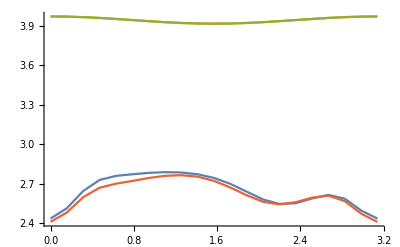

```mathematica
ListLinePlot[{rd264mean,rd264max,rd64max,rd64mean}]
```

```mathematica
ListPlot3D[Table[{n,rd264n[[n]]},{n,1,21}],PlotRange->All]
```

ListPlot3D::arrayerr: {{1.,{0.,2.,3.97223,2.22631,0.644267,2.17116,3.79447,2.39552,1.12406,2.35776,3.69278,2.66939,1.78282,2.36817,3.2326,«22»,2.03984,2.78361,2.41652,1.60948,1.95842,2.70644,2.3094,1.73374,2.26884,2.52216,2.57003,2.28368,2.13938,«450»}},«19»,«1»} must be a valid array or a list of valid arrays.

ListPlot3D[{{1,{0.,2.,3.9722344602909474,2.22631282626999028,0.644266660562906046,2.17115513046160524,3.79446673366500065,487,2.87384685212547097,3.15987045462203486,2.32404493724410788,2.23855961632775991,3.19234046876350552,3.19440560206493629}},19,{21,{1}}},1]
 |  |  |  |

```mathematica
Table[RudinShapiro[n],{n,0,1000}]
```

{1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,1,1,1,-1,1,1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,-1,-1,-1,1,-1,-1,1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,1,1,-1,1,1,-1,1,1}

## All plots

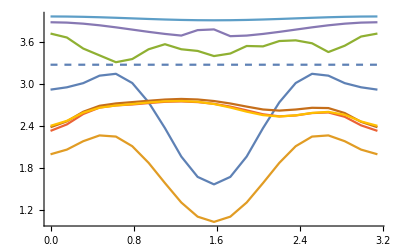

```mathematica
Show[Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],ListLinePlot[{rdnmax,rdmean,rd16max,rd16mean,rd32max,rd32mean,rd64max,rd64mean}],PlotRange->All]
```

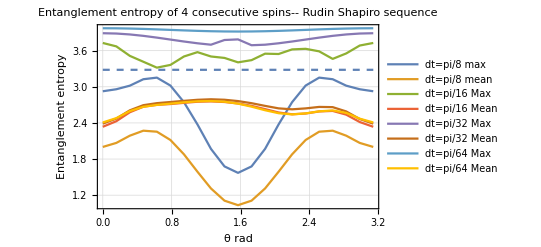

```mathematica
Show[ListLinePlot[{rdnmax,rdmean,rd16max,rd16mean,rd32max,rd32mean,rd64max,rd64mean},PlotTheme->"Detailed",PlotLegends->Placed[{"dt=pi/8 max","dt=pi/8 mean ","dt=pi/16 Max","dt=pi/16 Mean","dt=pi/32 Max","dt=pi/32 Mean","dt=pi/64 Max","dt=pi/64 Mean"},{0.8,0.2}]],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],PlotRange->All,FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[θ rad],None}},PlotLabel->HoldForm[Entanglement entropy of 4 consecutive spins -- Rudin Shapiro sequence],LabelStyle->{FontFamily->"TeX Gyre Pagella",RGBColor[0.,0.,0.]},LabelStyle->{17,GrayLevel[0]}]
```

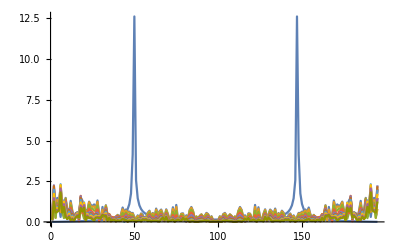

```mathematica
Show[ListLinePlot[Abs[Fourier[Table[normal3[[n]]-2,{n,1,Dimensions[normal3][[1]]-5}]]],PlotRange->All],ListLinePlot[Table[Abs[Fourier[Table[Drop[rdn[[m]],5][[n]]-rdmean[[m]][[2]],{n,1,195}]]],{m,1,10}],PlotRange->All]]
```

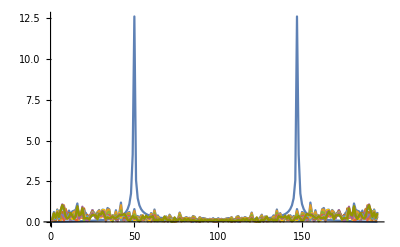

```mathematica
Show[ListLinePlot[Abs[Fourier[Table[normal3[[n]]-2,{n,1,Dimensions[normal3][[1]]-5}]]],PlotRange->All],ListLinePlot[Table[Abs[Fourier[Table[Drop[rd16n[[m]],5][[n]]-rd16mean[[m]][[2]],{n,1,195}]]],{m,1,10}],PlotRange->All]]
```

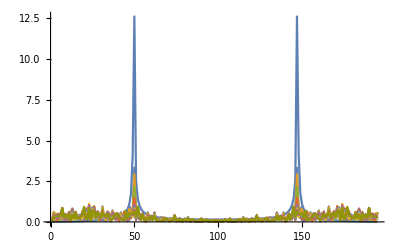

```mathematica
Show[ListLinePlot[Abs[Fourier[Table[normal3[[n]]-2,{n,1,Dimensions[normal3][[1]]-5}]]],PlotRange->All],ListLinePlot[Table[Abs[Fourier[Table[Drop[rd32n[[m]],5][[n]]-rd32mean[[m]][[2]],{n,1,195}]]],{m,1,10}],PlotRange->All]]
```

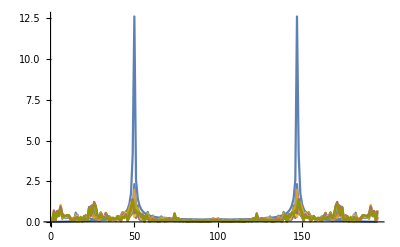

```mathematica
Show[ListLinePlot[Abs[Fourier[Table[normal3[[n]]-2,{n,1,Dimensions[normal3][[1]]-5}]]],PlotRange->All],ListLinePlot[Table[Abs[Fourier[Table[Drop[rd64n[[m]],5][[n]]-rd64mean[[m]][[2]],{n,1,195}]]],{m,1,10}],PlotRange->All]]
```

Part::partd: Part specification fibon⟦1⟧ is longer than depth of object.

Drop::drop: Cannot drop positions 1 through 5 in fibon⟦1⟧.

Part::partd: Part specification fibomean⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of Drop[fibon⟦1⟧,5] does not exist.

Part::partw: Part 4 of Drop[fibon⟦1⟧,5] does not exist.

Part::partw: Part 5 of Drop[fibon⟦1⟧,5] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Fourier::fftl: Argument … is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument {-1.+fibon⟦1⟧,4.,-1.+Drop[fibon⟦1⟧,5]⟦3⟧,-1.+Drop[fibon⟦1⟧,5]⟦4⟧,-1.+Drop[fibon⟦1⟧,5]⟦5⟧,-1.+Drop[fibon⟦1⟧,5]⟦6⟧,-1.+Drop[fibon⟦1⟧,5]⟦7⟧,-1.+Drop[fibon⟦1⟧,5]⟦8⟧,-1.+Drop[fibon⟦1⟧,5]⟦9⟧,-1.+Drop[fibon⟦1⟧,5]⟦10⟧,-1.+Drop[fibon⟦1⟧,5]⟦11⟧,-1.+Drop[fibon⟦1⟧,5]⟦12⟧,«28»,-1.+Drop[fibon⟦1⟧,5]⟦41⟧,-1.+Drop[fibon⟦1⟧,5]⟦42⟧,-1.+Drop[fibon⟦1⟧,5]⟦43⟧,-1.+Drop[fibon⟦1⟧,5]⟦44⟧,-1.+Drop[fibon⟦1⟧,5]⟦45⟧,-1.+Drop[fibon⟦1⟧,5]⟦46⟧,-1.+Drop[fibon⟦1⟧,5]⟦47⟧,-1.+Drop[fibon⟦1⟧,5]⟦48⟧,-1.+Drop[fibon⟦1⟧,5]⟦49⟧,-1.+Drop[fibon⟦1⟧,5]⟦50⟧,«55»} is not a non-empty list or rectangular array of numeric quantities.

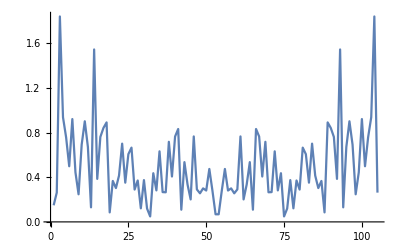

```mathematica
ListLinePlot[{Abs[Fourier[Table[Drop[rdn[[1]],5][[n]]-rdmean[[1]][[2]],{n,1,105}]]],Abs[Fourier[Table[Drop[fibon[[1]],5][[n]]-fibomean[[1]][[2]],{n,1,105}]]]},PlotRange->All]
```

Part::partd: Part specification fibon⟦10⟧ is longer than depth of object.

Drop::drop: Cannot drop positions 1 through 5 in fibon⟦10⟧.

Part::partd: Part specification fibomean⟦10⟧ is longer than depth of object.

Part::partw: Part 3 of Drop[fibon⟦10⟧,5] does not exist.

Part::partw: Part 4 of Drop[fibon⟦10⟧,5] does not exist.

Part::partw: Part 5 of Drop[fibon⟦10⟧,5] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Fourier::fftl: Argument {-10+fibon⟦10⟧,-5,-10+Drop[fibon⟦10⟧,5]⟦3⟧,-10+Drop[fibon⟦10⟧,5]⟦4⟧,-10+Drop[fibon⟦10⟧,5]⟦5⟧,-10+Drop[fibon⟦10⟧,5]⟦6⟧,-10+Drop[fibon⟦10⟧,5]⟦7⟧,-10+Drop[fibon⟦10⟧,5]⟦8⟧,-10+Drop[fibon⟦10⟧,5]⟦9⟧,-10+Drop[fibon⟦10⟧,5]⟦10⟧,-10+Drop[fibon⟦10⟧,5]⟦11⟧,-10+Drop[fibon⟦10⟧,5]⟦12⟧,«28»,-10+Drop[fibon⟦10⟧,5]⟦41⟧,-10+Drop[fibon⟦10⟧,5]⟦42⟧,-10+Drop[fibon⟦10⟧,5]⟦43⟧,-10+Drop[fibon⟦10⟧,5]⟦44⟧,-10+Drop[fibon⟦10⟧,5]⟦45⟧,-10+Drop[fibon⟦10⟧,5]⟦46⟧,-10+Drop[fibon⟦10⟧,5]⟦47⟧,-10+Drop[fibon⟦10⟧,5]⟦48⟧,-10+Drop[fibon⟦10⟧,5]⟦49⟧,-10+Drop[fibon⟦10⟧,5]⟦50⟧,«55»} is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument {-10.+fibon⟦10⟧,-5.,-10.+Drop[fibon⟦10⟧,5]⟦3⟧,-10.+Drop[fibon⟦10⟧,5]⟦4⟧,-10.+Drop[fibon⟦10⟧,5]⟦5⟧,-10.+Drop[fibon⟦10⟧,5]⟦6⟧,-10.+Drop[fibon⟦10⟧,5]⟦7⟧,-10.+Drop[fibon⟦10⟧,5]⟦8⟧,-10.+Drop[fibon⟦10⟧,5]⟦9⟧,-10.+Drop[fibon⟦10⟧,5]⟦10⟧,-10.+Drop[fibon⟦10⟧,5]⟦11⟧,«30»,-10.+Drop[fibon⟦10⟧,5]⟦42⟧,-10.+Drop[fibon⟦10⟧,5]⟦43⟧,-10.+Drop[fibon⟦10⟧,5]⟦44⟧,-10.+Drop[fibon⟦10⟧,5]⟦45⟧,-10.+Drop[fibon⟦10⟧,5]⟦46⟧,-10.+Drop[fibon⟦10⟧,5]⟦47⟧,-10.+Drop[fibon⟦10⟧,5]⟦48⟧,-10.+Drop[fibon⟦10⟧,5]⟦49⟧,-10.+Drop[fibon⟦10⟧,5]⟦50⟧,«55»} is not a non-empty list or rectangular array of numeric quantities.

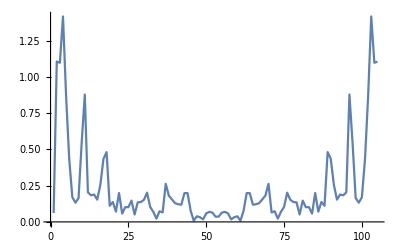

```mathematica
ListLinePlot[{Abs[Fourier[Table[Drop[rdn[[10]],5][[n]]-rdmean[[10]][[2]],{n,1,105}]]],Abs[Fourier[Table[Drop[fibon[[10]],5][[n]]-fibomean[[10]][[2]],{n,1,105}]]]},PlotRange->All]
```

```mathematica
normal2={-0.,2.,4.,2.,-0.,2.,4.,2.,-0.,2.,4.,2.,-0.,2.,4.,2.,-0.,2.,4.,2.,-0.,2.,4.,2.,-0.,2.,4.,2.,-0.,2.,4.,2.,-0.,2.,4.,2.,-0.,2.,4.,2.}
```

{0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.}

```mathematica
Dimensions[normal2]
```

{40}

```mathematica
normal3=Flatten[{normal2,normal2,normal2,normal2,normal2}]
```

{0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.,0.,2.,4.,2.}

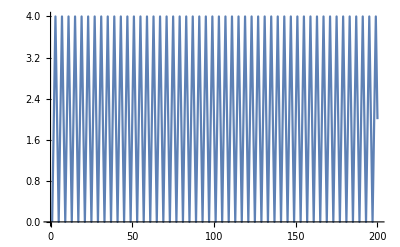

```mathematica
ListLinePlot[normal3]
```

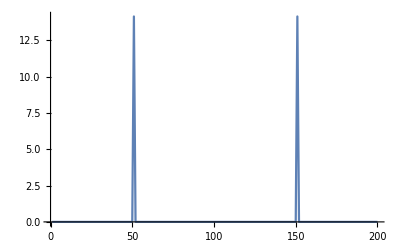

```mathematica
ListLinePlot[Abs[Fourier[Table[normal3[[n]]-2,{n,1,Dimensions[normal3][[1]]}]]],PlotRange->All]
```

## kicked interaction term

## dt = pi/8

### data

```mathematica
datars8={-0.000000000000000000*10^+00,1.201752073385713215*10^+00,1.404764034988925214*10^+00,1.624883029461678507*10^+00,1.404764034988924992*10^+00,1.624883029461680284*10^+00,1.593851164854310110*10^+00,1.624883029461683837*10^+00,1.593851164854312996*10^+00,8.216731072033693906*10^-01,1.290544393841772663*10^+00,4.495892585821257281*10^-01,1.290544393841771775*10^+00,8.216731072033656158*10^-01,1.593851164854312996*10^+00,8.216731072033632843*10^-01,1.593851164854311442*10^+00,8.216731072033612859*10^-01,1.290544393841767334*10^+00,4.495892585821152365*10^-01,1.290544393841766224*10^+00,4.495892585821136267*10^-01,1.171533725585266250*10^+00,4.495892585821138487*10^-01,1.171533725585268026*10^+00,4.495892585821140708*10^-01,1.290544393841771331*10^+00,8.216731072033500727*10^-01,1.290544393841772441*10^+00,4.495892585821127940*10^-01,1.171533725585268249*10^+00,4.495892585821112397*10^-01,1.171533725585269137*10^+00,1.700309114777328823*10^+00,1.273741385706505636*10^+00,1.435086477961448725*10^+00,1.273741385706507856*10^+00,1.435086477961450058*10^+00,7.942844088298023353*10^-01,1.435086477961448503*10^+00,7.942844088297975613*10^-01,1.574682138150331312*10^+00,1.004172845183168183*10^+00,8.407056156422205717*10^-01,1.004172845183168405*10^+00,1.574682138150338861*10^+00,7.942844088297961180*10^-01,1.574682138150340416*10^+00,7.942844088297940086*10^-01,1.435086477961449392*10^+00,1.273741385706503415*10^+00,1.700309114777342145*10^+00,1.273741385706501639*10^+00,1.700309114777342145*10^+00,1.171533725585272023*10^+00,1.700309114777344366*10^+00,1.171533725585274022*10^+00,1.700309114777347475*10^+00,1.273741385706499862*10^+00,1.435086477961448281*10^+00,1.273741385706500528*10^+00,1.700309114777349473*10^+00,1.171533725585276908*10^+00,1.700309114777352359*10^+00,1.171533725585278241*10^+00,1.700309114777354802*10^+00,1.273741385706496976*10^+00,1.435086477961449392*10^+00,1.273741385706497864*10^+00,1.435086477961450946*10^+00,7.942844088297628113*10^-01,1.435086477961448725*10^+00,7.942844088297571492*10^-01,1.574682138150342414*10^+00,1.004172845183171958*10^+00,8.407056156422076931*10^-01,1.004172845183171958*10^+00,1.574682138150350408*10^+00,7.942844088297529304*10^-01,1.574682138150352184*10^+00,7.942844088297529304*10^-01,1.574682138150352850*10^+00,1.004172845183177065*10^+00,8.407056156422020310*10^-01,1.004172845183177509*10^+00,8.407056156422012538*10^-01,1.573483708331512521*10^+00,8.407056156422034743*10^-01,1.573483708331514075*10^+00,8.407056156422054727*10^-01,1.004172845183180396*10^+00,1.574682138150369060*10^+00,1.004172845183181950*10^+00,8.407056156422045845*10^-01,1.573483708331522068*10^+00,8.407056156422054727*10^-01,1.573483708331520736*10^+00,8.407056156422063609*10^-01,1.004172845183183282*10^+00,1.574682138150379718*10^+00,1.004172845183184393*10^+00,1.574682138150381938*10^+00,7.942844088297382754*10^-01,1.574682138150382826*10^+00,7.942844088297371652*10^-01,1.435086477961468487*10^+00,1.273741385706503859*10^+00,1.700309114777406982*10^+00,1.273741385706500306*10^+00,1.435086477961466489*10^+00,7.942844088297241756*10^-01,1.435086477961464269*10^+00,7.942844088297195126*10^-01,1.574682138150378607*10^+00,1.004172845183182616*10^+00,8.407056156421931492*10^-01,1.004172845183183060*10^+00,8.407056156421927051*10^-01,1.573483708331529840*10^+00,8.407056156421945925*10^-01,1.573483708331531616*10^+00,8.407056156421965909*10^-01,1.004172845183184837*10^+00,1.574682138150393929*10^+00,1.004172845183185503*10^+00,8.407056156421943705*10^-01,1.573483708331538500*10^+00,8.407056156421948145*10^-01,1.573483708331539388*10^+00,8.025282191918992059*10^-01,1.516506993800313730*10^+00,1.299173967532606611*10^+00,1.516506993800313730*10^+00,1.299173967532607277*10^+00,1.588692277252855778*10^+00,1.299173967532606833*10^+00,1.588692277252854890*10^+00,1.223541710382062941*10^+00,2.808572368303369204*10^-01,1.273880544614204080*10^+00,2.808572368303340339*10^-01,1.223541710382064496*10^+00,1.588692277252861107*10^+00,1.223541710382065384*10^+00,1.588692277252863994*10^+00,1.223541710382067160*10^+00,2.808572368303264288*10^-01,1.273880544614206078*10^+00,2.808572368303240419*10^-01,1.273880544614205412*10^+00,1.067643082990746617*10^+00,1.273880544614202748*10^+00,1.067643082990742176*10^+00,1.273880544614200971*10^+00,2.808572368303126621*10^-01,1.223541710382064274*10^+00,2.808572368303088873*10^-01,1.273880544614201415*10^+00,1.067643082990735515*10^+00,1.273880544614200083*10^+00,1.067643082990733516*10^+00,1.717197516560161397*10^+00,1.542862855958187840*10^+00,1.171833367822168404*10^+00,1.542862855958186508*10^+00,1.171833367822167293*10^+00,1.201319257815546049*10^+00,1.171833367822167293*10^+00,1.201319257815546715*10^+00,1.029728895710616404*10^-01,1.201771017359981153*10^+00,1.596379878909021333*10^+00,1.201771017359980931*10^+00,1.029728895710562281*10^-01,1.201319257815545383*10^+00,1.029728895710520925*10^-01,1.201319257815543384*10^+00,1.171833367822158856*10^+00,1.542862855958187840*10^+00,1.717197516560178716*10^+00,1.542862855958191837*10^+00,1.717197516560183379*10^+00,1.067643082990724634*10^+00,1.717197516560185822*10^+00,1.067643082990723746*10^+00,1.717197516560188486*10^+00,1.542862855958203605*10^+00,1.171833367822155081*10^+00,1.542862855958203383*10^+00,1.717197516560196924*10^+00,1.067643082990724412*10^+00,1.717197516560199588*10^+00,1.067643082990725301*10^+00,1.273880544614193866*10^+00,2.808572368302271749*10^-01,1.223541710382073600*10^+00,2.808572368302229560*10^-01,1.223541710382072267*10^+00,1.588692277252894414*10^+00,1.223541710382073822*10^+00,2.722912528242654327*10^-14,1.157960598926154550*10^+00,1.354187576380417868*10^+00,1.600940457377419079*10^+00,1.354187576380418090*10^+00,1.600940457377419079*10^+00,1.627287299271850785*10^+00,1.600940457377423742*10^+00,1.627287299271854781*10^+00,9.471409948758758857*10^-01,1.381424898542072732*10^+00,6.117533077140023812*10^-01,1.381424898542072732*10^+00,9.471409948758715558*10^-01,1.627287299271852783*10^+00,9.471409948758671149*10^-01,1.627287299271853005*10^+00,9.471409948758640063*10^-01,1.381424898542066959*10^+00,6.117533077139862829*10^-01,1.381424898542066293*10^+00,6.117533077139847286*10^-01,1.276055676427993779*10^+00,6.117533077139847286*10^-01,1.276055676427995111*10^+00,6.117533077139846176*10^-01,1.381424898542072510*10^+00,9.471409948758504616*10^-01,1.381424898542073620*10^+00,6.117533077139812869*10^-01,1.276055676427994667*10^+00,6.117533077139810649*10^-01,1.276055676427996222*10^+00,1.648359785954874424*10^+00,1.239541052132860255*10^+00,1.429661395172592941*10^+00,1.239541052132860255*10^+00,1.429661395172593608*10^+00,7.484305579238342832*10^-01,1.429661395172591387*10^+00,7.484305579238308415*10^-01,1.516617465218512040*10^+00,1.018286735112380992*10^+00,9.167665905747025556*10^-01,1.018286735112380104*10^+00,1.516617465218517591*10^+00,7.484305579238290651*10^-01,1.516617465218518701*10^+00,7.484305579238283990*10^-01,1.429661395172592719*10^+00,1.239541052132859811*10^+00,1.648359785954884860*10^+00,1.239541052132855814*10^+00,1.648359785954882639*10^+00,1.276055676427998442*10^+00,1.648359785954883749*10^+00,1.276055676428000663*10^+00,1.648359785954886192*10^+00,1.239541052132853372*10^+00,1.429661395172589833*10^+00,1.239541052132854038*10^+00,1.648359785954887080*10^+00,1.276055676428002439*10^+00,1.648359785954890189*10^+00,1.276055676428004881*10^+00,1.648359785954892187*10^+00,1.239541052132853372*10^+00,1.429661395172590499*10^+00,1.239541052132854038*10^+00,1.429661395172592053*10^+00,7.484305579237950923*10^-01,1.429661395172589167*10^+00,7.484305579237895412*10^-01,1.516617465218517147*10^+00,1.018286735112385877*10^+00,9.167665905746995580*10^-01,1.018286735112385655*10^+00,1.516617465218524252*10^+00,7.484305579237847672*10^-01,1.516617465218523808*10^+00,7.484305579237842121*10^-01,1.516617465218526917*10^+00,1.018286735112388763*10^+00,9.167665905746933408*10^-01,1.018286735112388319*10^+00,9.167665905746933408*10^-01,1.566276817892270135*10^+00,9.167665905746947841*10^-01,1.566276817892271911*10^+00,9.167665905746977817*10^-01,1.018286735112391650*10^+00,1.516617465218540239*10^+00,1.018286735112390762*10^+00,9.167665905746941180*10^-01,1.566276817892276796*10^+00,9.167665905746951172*10^-01,1.566276817892278350*10^+00,9.167665905746958943*10^-01,1.018286735112392316*10^+00,1.516617465218548455*10^+00,1.018286735112393648*10^+00,1.516617465218550453*10^+00,7.484305579237646722*10^-01,1.516617465218552230*10^+00,7.484305579237631179*10^-01,1.429661395172606042*10^+00,1.239541052132856702*10^+00,1.648359785954941481*10^+00,1.239541052132854926*10^+00,1.429661395172604932*10^+00,7.484305579237503503*10^-01,1.429661395172603378*10^+00,7.484305579237471306*10^-01,1.516617465218546901*10^+00,1.018286735112392982*10^+00,9.167665905746857913*10^-01,1.018286735112391872*10^+00,9.167665905746851251*10^-01,1.566276817892285900*10^+00,9.167665905746869015*10^-01,1.566276817892287454*10^+00,9.167665905746890109*10^-01,1.018286735112392538*10^+00,1.516617465218560001*10^+00,1.018286735112394759*10^+00,9.167665905746881228*10^-01,1.566276817892293449*10^+00,9.167665905746890109*10^-01,1.566276817892295670*10^+00,8.822957320729510888*10^-01,1.524034925008741492*10^+00,1.395264504262554439*10^+00,1.524034925008741492*10^+00,1.395264504262556216*10^+00,1.631038888904518869*10^+00,1.395264504262556660*10^+00,1.631038888904519535*10^+00,1.252647916630875713*10^+00,4.005904579170867508*10^-01,1.310489617419861919*10^+00,4.005904579170844193*10^-01,1.252647916630876601*10^+00,1.631038888904526418*10^+00,1.252647916630877933*10^+00,1.631038888904529971*10^+00,1.252647916630878822*10^+00,4.005904579170774249*10^-01,1.310489617419862363*10^+00,4.005904579170747049*10^-01,1.310489617419862807*10^+00,1.021394426799560051*10^+00,1.310489617419861030*10^+00,1.021394426799558275*10^+00,1.310489617419859920*10^+00,4.005904579170671553*10^-01,1.252647916630877489*10^+00,4.005904579170649904*10^-01,1.310489617419859920*10^+00,1.021394426799553612*10^+00,1.310489617419858588*10^+00,1.021394426799550281*10^+00,1.686109769196044272*10^+00,1.598566912232080028*10^+00,1.272358964556135064*10^+00,1.598566912232079140*10^+00,1.272358964556133065*10^+00,1.297838058333266487*10^+00,1.272358964556134175*10^+00,1.297838058333268041*10^+00,2.714670737929079647*10^-01,1.279108758236836119*10^+00,1.628956799245516507*10^+00,1.279108758236835897*10^+00,2.714670737929039124*10^-01,1.297838058333267153*10^+00,2.714670737928981392*10^-01,1.297838058333264932*10^+00,1.272358964556128846*10^+00,1.598566912232081361*10^+00,1.686109769196058039*10^+00,1.598566912232085135*10^+00,1.686109769196061592*10^+00,1.021394426799537181*10^+00,1.686109769196064256*10^+00,1.021394426799534294*10^+00,1.686109769196064923*10^+00,1.598566912232094239*10^+00,1.272358964556123739*10^+00,1.598566912232093351*10^+00,1.686109769196072694*10^+00,1.021394426799531852*10^+00,1.686109769196074470*10^+00,1.021394426799530519*10^+00,1.310489617419845487*10^+00,4.005904579169823898*10^-01,1.252647916630880820*10^+00,4.005904579169788371*10^-01,1.252647916630879266*10^+00,1.631038888904562834*10^+00,1.252647916630882152*10^+00,-9.610279511444755881*10^-16,1.033390542523312750*10^+00,1.221949211164785387*10^+00,1.535324982625515977*10^+00,1.221949211164784055*10^+00,1.535324982625514867*10^+00,1.690624636963503402*10^+00,1.535324982625518198*10^+00,1.690624636963506955*10^+00,1.193393155189223620*10^+00,1.492742957808428139*10^+00,9.602870581271540917*10^-01,1.492742957808427917*10^+00,1.193393155189218513*10^+00,1.690624636963507843*10^+00,1.193393155189216071*10^+00,1.690624636963507843*10^+00,1.193393155189216293*10^+00,1.492742957808425253*10^+00,9.602870581271440997*10^-01,1.492742957808423032*10^+00,9.602870581271405470*10^-01,1.460892347312863659*10^+00,9.602870581271413242*10^-01,1.460892347312865880*10^+00,9.602870581271409911*10^-01,1.492742957808430138*10^+00,1.193393155189206079*10^+00,1.492742957808430138*10^+00,9.602870581271414352*10^-01,1.460892347312866546*10^+00,9.602870581271414352*10^-01,1.460892347312867656*10^+00,1.581581842653898118*10^+00,1.254477586730408767*10^+00,1.463402689591171146*10^+00,1.254477586730408323*10^+00,1.463402689591173589*10^+00,7.060262793902718492*10^-01,1.463402689591169592*10^+00,7.060262793902674083*10^-01,1.445815846543477612*10^+00,1.133247279526737206*10^+00,1.130328214970775624*10^+00,1.133247279526737428*10^+00,1.445815846543482053*10^+00,7.060262793902642997*10^-01,1.445815846543483385*10^+00,7.060262793902623013*10^-01,1.463402689591170480*10^+00,1.254477586730402994*10^+00,1.581581842653904779*10^+00,1.254477586730401661*10^+00,1.581581842653903891*10^+00,1.460892347312872541*10^+00,1.581581842653905445*10^+00,1.460892347312875206*10^+00,1.581581842653907666*10^+00,1.254477586730401439*10^+00,1.463402689591170480*10^+00,1.254477586730402550*10^+00,1.581581842653908110*10^+00,1.460892347312878981*10^+00,1.581581842653910330*10^+00,1.460892347312881201*10^+00,1.581581842653913439*10^+00,1.254477586730401661*10^+00,1.463402689591171146*10^+00,1.254477586730403882*10^+00,1.463402689591173367*10^+00,7.060262793902365441*10^-01,1.463402689591169148*10^+00,7.060262793902301048*10^-01,1.445815846543477612*10^+00,1.133247279526742535*10^+00,1.130328214970775402*10^+00,1.133247279526742091*10^+00,1.445815846543483607*10^+00,7.060262793902259970*10^-01,1.445815846543484939*10^+00,7.060262793902247758*10^-01,1.445815846543484717*10^+00,1.133247279526746754*10^+00,1.130328214970771405*10^+00,1.133247279526746976*10^+00,1.130328214970771405*10^+00,1.596519051282925261*10^+00,1.130328214970772738*10^+00,1.596519051282926149*10^+00,1.130328214970773404*10^+00,1.133247279526748086*10^+00,1.445815846543495375*10^+00,1.133247279526747420*10^+00,1.130328214970771405*10^+00,1.596519051282932811*10^+00,1.130328214970772738*10^+00,1.596519051282935475*10^+00,1.130328214970774292*10^+00,1.133247279526748974*10^+00,1.445815846543501593*10^+00,1.133247279526750084*10^+00,1.445815846543502481*10^+00,7.060262793902041256*10^-01,1.445815846543503369*10^+00,7.060262793902027934*10^-01,1.463402689591179806*10^+00,1.254477586730396999*10^+00,1.581581842653949188*10^+00,1.254477586730395888*10^+00,1.463402689591178030*10^+00,7.060262793901914691*10^-01,1.463402689591176475*10^+00,7.060262793901855849*10^-01,1.445815846543498040*10^+00,1.133247279526748086*10^+00,1.130328214970767409*10^+00,1.133247279526746754*10^+00,1.130328214970765854*10^+00,1.596519051282945689*10^+00,1.130328214970767409*10^+00,1.596519051282946355*10^+00,1.130328214970768741*10^+00,1.133247279526749196*10^+00,1.445815846543508254*10^+00,1.133247279526749640*10^+00,1.130328214970767409*10^+00,1.596519051282951240*10^+00,1.130328214970768963*10^+00,1.596519051282953017*10^+00,1.084405507449651473*10^+00,1.562623150609918632*10^+00,1.598574993529521038*10^+00,1.562623150609918410*10^+00,1.598574993529521704*10^+00,1.755905476986594271*10^+00,1.598574993529522370*10^+00,1.755905476986596270*10^+00,1.393735098407433481*10^+00,7.149647377033576667*10^-01,1.398243552957670666*10^+00,7.149647377033547802*10^-01,1.393735098407433037*10^+00,1.755905476986602709*10^+00,1.393735098407434592*10^+00,1.755905476986607372*10^+00,1.393735098407437034*10^+00,7.149647377033488960*10^-01,1.398243552957672220*10^+00,7.149647377033476747*10^-01,1.398243552957672886*10^+00,9.778714725567162480*10^-01,1.398243552957670666*10^+00,9.778714725567124733*10^-01,1.398243552957669777*10^+00,7.149647377033403473*10^-01,1.393735098407435702*10^+00,7.149647377033379048*10^-01,1.398243552957670666*10^+00,9.778714725567067001*10^-01,1.398243552957670222*10^+00,9.778714725567039245*10^-01,1.690208214598873049*10^+00,1.752834798814287831*10^+00,1.531496463050983525*10^+00,1.752834798814286943*10^+00,1.531496463050982415*10^+00,1.515754643745135244*10^+00,1.531496463050983081*10^+00,1.515754643745136354*10^+00,6.719551458981365410*10^-01,1.394677335377644489*10^+00,1.707631098803494840*10^+00,1.394677335377643823*10^+00,6.719551458981327663*10^-01,1.515754643745136132*10^+00,6.719551458981292136*10^-01,1.515754643745134578*10^+00,1.531496463050979528*10^+00,1.752834798814287831*10^+00,1.690208214598882597*10^+00,1.752834798814292938*10^+00,1.690208214598885039*10^+00,9.778714725566876043*10^-01,1.690208214598888148*10^+00,9.778714725566854948*10^-01,1.690208214598890368*10^+00,1.752834798814305151*10^+00,1.531496463050978418*10^+00,1.752834798814304484*10^+00,1.690208214598893033*10^+00,9.778714725566827193*10^-01,1.690208214598894587*10^+00,9.778714725566808319*10^-01,1.398243552957664448*10^+00,7.149647377032686268*10^-01,1.393735098407440587*10^+00,7.149647377032648521*10^-01,1.393735098407438810*10^+00,1.755905476986644009*10^+00,1.393735098407440365*10^+00,9.610279511444749964*10^-16,8.474263344968484546*10^-01,1.054831036137992006*10^+00,1.486339494964284746*10^+00,1.054831036137991118*10^+00,1.486339494964285635*10^+00,1.722189931713457911*10^+00,1.486339494964289631*10^+00,1.722189931713461242*10^+00,1.480923794119043402*10^+00,1.616538443860544128*10^+00,1.304112293644610343*10^+00,1.616538443860543017*10^+00,1.480923794119040737*10^+00,1.722189931713459465*10^+00,1.480923794119040737*10^+00,1.722189931713461686*10^+00,1.480923794119039627*10^+00,1.616538443860541019*10^+00,1.304112293644602349*10^+00,1.616538443860539687*10^+00,1.304112293644598575*10^+00,1.638199709963369832*10^+00,1.304112293644600795*10^+00,1.638199709963373163*10^+00,1.304112293644602794*10^+00,1.616538443860545460*10^+00,1.480923794119036518*10^+00,1.616538443860547014*10^+00,1.304112293644601683*10^+00,1.638199709963375827*10^+00,1.304112293644602572*10^+00,1.638199709963378936*10^+00,1.646292484561461489*10^+00,1.480233277618920873*10^+00,1.600570145905266140*10^+00,1.480233277618921539*10^+00,1.600570145905267694*10^+00,7.861499049313974696*10^-01,1.600570145905266362*10^+00,7.861499049313945831*10^-01,1.517477423093693378*10^+00,1.358557776299879505*10^+00,1.411547593009242263*10^+00,1.358557776299877506*10^+00,1.517477423093697375*10^+00,7.861499049313880327*10^-01,1.517477423093697375*10^+00,7.861499049313878107*10^-01,1.600570145905266806*10^+00,1.480233277618916210*10^+00,1.646292484561467706*10^+00,1.480233277618913990*10^+00,1.646292484561465930*10^+00,1.638199709963387374*10^+00,1.646292484561467262*10^+00,1.638199709963388928*10^+00,1.646292484561468816*10^+00,1.480233277618911547*10^+00,1.600570145905267028*10^+00,1.480233277618911769*10^+00,1.646292484561468372*10^+00,1.638199709963393591*10^+00,1.646292484561470371*10^+00,1.638199709963394701*10^+00,1.646292484561471259*10^+00,1.480233277618908883*10^+00,1.600570145905267028*10^+00,1.480233277618908216*10^+00,1.600570145905268582*10^+00,7.861499049313634968*10^-01,1.600570145905265029*10^+00,7.861499049313596110*10^-01,1.517477423093694044*10^+00,1.358557776299879727*10^+00,1.411547593009240265*10^+00,1.358557776299877951*10^+00,1.517477423093699151*10^+00,7.861499049313562804*10^-01,1.517477423093699596*10^+00,7.861499049313553922*10^-01,1.517477423093701372*10^+00,1.358557776299884168*10^+00,1.411547593009238932*10^+00,1.358557776299884168*10^+00,1.411547593009239154*10^+00,1.667785277755078344*10^+00,1.411547593009239598*10^+00,1.667785277755078566*10^+00,1.411547593009241153*10^+00,1.358557776299885056*10^+00,1.517477423093708477*10^+00,1.358557776299886388*10^+00,1.411547593009241153*10^+00,1.667785277755084561*10^+00,1.411547593009243373*10^+00,1.667785277755086559*10^+00,1.411547593009244483*10^+00,1.358557776299887498*10^+00,1.517477423093714251*10^+00,1.358557776299891495*10^+00,1.517477423093717803*10^+00,7.861499049313439569*10^-01,1.517477423093716915*10^+00,7.861499049313418475*10^-01,1.600570145905273911*10^+00,1.480233277618898668*10^+00,1.646292484561493463*10^+00,1.480233277618896892*10^+00,1.600570145905274577*10^+00,7.861499049313324106*10^-01,1.600570145905272135*10^+00,7.861499049313296350*10^-01,1.517477423093712918*10^+00,1.358557776299886832*10^+00,1.411547593009239598*10^+00,1.358557776299885500*10^+00,1.411547593009239598*10^+00,1.667785277755094109*10^+00,1.411547593009240487*10^+00,1.667785277755093887*10^+00,1.411547593009241153*10^+00,1.358557776299885500*10^+00,1.517477423093719135*10^+00,1.358557776299887276*10^+00,1.411547593009240043*10^+00,1.667785277755099660*10^+00,1.411547593009242263*10^+00,1.667785277755100104*10^+00,1.385321852002250775*10^+00,1.650376973447484019*10^+00,1.784559887012042267*10^+00,1.650376973447484241*10^+00,1.784559887012042712*10^+00,1.907324393396041984*10^+00,1.784559887012043600*10^+00,1.907324393396042872*10^+00,1.677340426999892609*10^+00,1.075022185769533456*10^+00,1.542065238009821204*10^+00,1.075022185769533234*10^+00,1.677340426999892831*10^+00,1.907324393396050422*10^+00,1.677340426999895051*10^+00,1.907324393396053308*10^+00,1.677340426999897716*10^+00,1.075022185769529681*10^+00,1.542065238009824091*10^+00,1.075022185769529237*10^+00,1.542065238009824979*10^+00,1.069881106766091161*10^+00,1.542065238009822536*10^+00,1.069881106766089385*10^+00,1.542065238009822759*10^+00,1.075022185769525240*10^+00,1.677340426999894829*10^+00,1.075022185769523464*10^+00,1.542065238009822981*10^+00,1.069881106766084944*10^+00,1.542065238009822314*10^+00,1.069881106766083390*10^+00,1.810767322034089410*10^+00,1.904714586047850267*10^+00,1.823078327542925425*10^+00,1.904714586047849822*10^+00,1.823078327542925425*10^+00,1.758639173457323901*10^+00,1.823078327542925425*10^+00,1.758639173457325677*10^+00,1.111728531367524919*10^+00,1.482582951465425625*10^+00,1.800382595822185738*10^+00,1.482582951465426069*10^+00,1.111728531367522477*10^+00,1.758639173457325677*10^+00,1.111728531367519590*10^+00,1.758639173457325455*10^+00,1.823078327542924537*10^+00,1.904714586047853153*10^+00,1.810767322034093851*10^+00,1.904714586047856262*10^+00,1.810767322034098958*10^+00,1.069881106766069401*10^+00,1.810767322034099847*10^+00,1.069881106766068957*10^+00,1.810767322034102289*10^+00,1.904714586047868474*10^+00,1.823078327542926758*10^+00,1.904714586047867364*10^+00,1.810767322034106508*10^+00,1.069881106766065404*10^+00,1.810767322034107618*10^+00,1.069881106766064072*10^+00,1.542065238009821648*10^+00,1.075022185769480165*10^+00,1.677340426999895939*10^+00,1.075022185769478167*10^+00,1.677340426999895495*10^+00,1.907324393396089057*10^+00,1.677340426999897716*10^+00,4.805139755722374982*10^-16,6.289791881778437066*10^-01,9.038853705994690513*10^-01,1.477065462886882008*10^+00,9.038853705994672749*10^-01,1.477065462886883562*10^+00,1.733455949730734913*10^+00,1.477065462886884228*10^+00,1.733455949730736689*10^+00,1.711733765382828176*10^+00,1.751258672372666858*10^+00,1.582003024577645522*10^+00,1.751258672372665082*10^+00,1.711733765382823513*10^+00,1.733455949730734691*10^+00,1.711733765382824179*10^+00,1.733455949730736245*10^+00,1.711733765382825734*10^+00,1.751258672372665304*10^+00,1.582003024577640415*10^+00,1.751258672372663083*10^+00,1.582003024577637973*10^+00,1.785375895893136722*10^+00,1.582003024577637973*10^+00,1.785375895893139830*10^+00,1.582003024577639749*10^+00,1.751258672372663749*10^+00,1.711733765382820183*10^+00,1.751258672372665082*10^+00,1.582003024577637751*10^+00,1.785375895893139830*10^+00,1.582003024577636641*10^+00,1.785375895893142273*10^+00,1.849809462360431533*10^+00,1.809787676485840935*10^+00,1.784218789616905720*10^+00,1.809787676485842933*10^+00,1.784218789616907053*10^+00,9.618037075433844008*10^-01,1.784218789616905276*10^+00,9.618037075433816252*10^-01,1.651671650066046881*10^+00,1.590038276368892944*10^+00,1.638385162727978184*10^+00,1.590038276368892944*10^+00,1.651671650066049546*10^+00,9.618037075433816252*10^-01,1.651671650066049546*10^+00,9.618037075433807370*10^-01,1.784218789616906164*10^+00,1.809787676485840935*10^+00,1.849809462360432422*10^+00,1.809787676485839381*10^+00,1.849809462360429757*10^+00,1.785375895893151821*10^+00,1.849809462360433976*10^+00,1.785375895893153153*10^+00,1.849809462360434864*10^+00,1.809787676485836272*10^+00,1.784218789616907275*10^+00,1.809787676485837382*10^+00,1.849809462360432866*10^+00,1.785375895893157150*10^+00,1.849809462360434642*10^+00,1.785375895893157150*10^+00,1.849809462360435752*10^+00,1.809787676485834274*10^+00,1.784218789616908829*10^+00,1.809787676485835384*10^+00,1.784218789616911494*10^+00,9.618037075433583105*10^-01,1.784218789616907053*10^+00,9.618037075433554239*10^-01,1.651671650066045549*10^+00,1.590038276368890946*10^+00,1.638385162727978628*10^+00,1.590038276368889170*10^+00,1.651671650066047103*10^+00,9.618037075433529814*10^-01,1.651671650066046215*10^+00,9.618037075433503169*10^-01,1.651671650066047992*10^+00,1.590038276368891168*10^+00,1.638385162727975519*10^+00,1.590038276368890280*10^+00,1.638385162727976185*10^+00,1.752824964302416744*10^+00,1.638385162727976851*10^+00,1.752824964302417188*10^+00,1.638385162727977518*10^+00,1.590038276368891612*10^+00,1.651671650066051988*10^+00,1.590038276368893833*10^+00,1.638385162727977518*10^+00,1.752824964302419852*10^+00,1.638385162727978184*10^+00,1.752824964302422295*10^+00,1.638385162727980404*10^+00,1.590038276368894277*10^+00,1.651671650066055097*10^+00,1.590038276368895609*10^+00,1.651671650066055097*10^+00,9.618037075433373273*10^-01,1.651671650066053987*10^+00,9.618037075433359950*10^-01,1.784218789616909717*10^+00,1.809787676485824282*10^+00,1.849809462360437973*10^+00,1.809787676485821839*10^+00,1.784218789616910605*10^+00,9.618037075433292227*10^-01,1.784218789616908829*10^+00,9.618037075433250038*10^-01,1.651671650066048880*10^+00,1.590038276368893833*10^+00,1.638385162727977962*10^+00,1.590038276368892944*10^+00,1.638385162727977740*10^+00,1.752824964302426514*10^+00,1.638385162727979294*10^+00,1.752824964302426514*10^+00,1.638385162727980404*10^+00,1.590038276368893388*10^+00,1.651671650066053321*10^+00,1.590038276368894721*10^+00,1.638385162727980848*10^+00,1.752824964302430732*10^+00,1.638385162727981736*10^+00,1.752824964302431621*10^+00,1.712255216635778288*10^+00,1.765848322120986857*10^+00,1.904977414474446684*10^+00,1.765848322120985969*10^+00,1.904977414474447350*10^+00,2.058469578806442435*10^+00,1.904977414474447128*10^+00,2.058469578806442879*10^+00,2.002645443809306425*10^+00,1.393088230444378128*10^+00,1.693734481042153295*10^+00,1.393088230444377462*10^+00,2.002645443809305981*10^+00,2.058469578806449096*10^+00,2.002645443809307757*10^+00,2.058469578806450873*10^+00,2.002645443809308645*10^+00,1.393088230444374354*10^+00,1.693734481042156403*10^+00,1.393088230444374132*10^+00,1.693734481042156848*10^+00,1.249893434541338166*10^+00,1.693734481042155515*10^+00,1.249893434541336834*10^+00,1.693734481042155737*10^+00,1.393088230444372133*10^+00,2.002645443809308645*10^+00,1.393088230444370801*10^+00,1.693734481042157514*10^+00,1.249893434541333503*10^+00,1.693734481042157292*10^+00,1.249893434541331727*10^+00,1.938118799430955441*10^+00,2.035279195471600300*10^+00,2.059748980415458064*10^+00,2.035279195471600744*10^+00,2.059748980415457176*10^+00,1.983816008746407178*10^+00,2.059748980415457620*10^+00,1.983816008746408288*10^+00,1.498574690788550656*10^+00,1.558191508606299625*10^+00,1.844179491319755559*10^+00,1.558191508606300513*10^+00,1.498574690788549324*10^+00,1.983816008746407400*10^+00,1.498574690788548658*10^+00,1.983816008746407178*10^+00,2.059748980415460728*10^+00,2.035279195471603408*10^+00,1.938118799430962103*10^+00,2.035279195471606517*10^+00,1.938118799430964101*10^+00,1.249893434541320847*10^+00,1.938118799430966765*10^+00,1.249893434541319293*10^+00,1.938118799430968764*10^+00,2.035279195471614955*10^+00,2.059748980415461617*10^+00,2.035279195471614067*10^+00,1.938118799430971650*10^+00,1.249893434541316850*10^+00,1.938118799430973649*10^+00,1.249893434541314852*10^+00,1.693734481042157292*10^+00,1.393088230444344156*10^+00,2.002645443809309977*10^+00,1.393088230444341935*10^+00,2.002645443809308645*10^+00,2.058469578806481515*10^+00,2.002645443809309977*10^+00,3.203426503814917641*10^-16,4.115261085513829409*10^-01,8.813230580469840758*10^-01,1.505257948120920286*10^+00,8.813230580469835207*10^-01,1.505257948120921618*10^+00,1.761054294362026429*10^+00,1.505257948120923617*10^+00,1.761054294362029760*10^+00,1.951314137955965533*10^+00,1.903347374701460870*10^+00,1.765912117735662479*10^+00,1.903347374701459982*10^+00,1.951314137955961980*10^+00,1.761054294362027317*10^+00,1.951314137955962202*10^+00,1.761054294362030204*10^+00,1.951314137955962202*10^+00,1.903347374701459538*10^+00,1.765912117735659592*10^+00,1.903347374701457317*10^+00,1.765912117735659370*10^+00,1.944470466543932519*10^+00,1.765912117735658926*10^+00,1.944470466543934517*10^+00,1.765912117735659148*10^+00,1.903347374701455763*10^+00,1.951314137955956429*10^+00,1.903347374701456651*10^+00,1.765912117735658482*10^+00,1.944470466543935405*10^+00,1.765912117735658260*10^+00,1.944470466543936737*10^+00,2.075211394106779572*10^+00,2.122142959505420201*10^+00,1.960632154589476928*10^+00,2.122142959505421089*10^+00,1.960632154589478704*10^+00,1.163845894300384876*10^+00,1.960632154589476484*10^+00,1.163845894300382877*10^+00,1.753215613742602708*10^+00,1.793960447295013028*10^+00,1.772392665324545202*10^+00,1.793960447295011029*10^+00,1.753215613742604928*10^+00,1.163845894300381989*10^+00,1.753215613742604262*10^+00,1.163845894300379324*10^+00,1.960632154589476261*10^+00,2.122142959505420201*10^+00,2.075211394106780460*10^+00,2.122142959505419313*10^+00,2.075211394106777796*10^+00,1.944470466543942955*10^+00,2.075211394106777796*10^+00,1.944470466543943399*10^+00,2.075211394106779128*10^+00,2.122142959505417537*10^+00,1.960632154589476706*10^+00,2.122142959505419757*10^+00,2.075211394106779572*10^+00,1.944470466543946729*10^+00,2.075211394106779572*10^+00,1.944470466543948284*10^+00,2.075211394106780460*10^+00,2.122142959505417981*10^+00,1.960632154589477150*10^+00,2.122142959505419313*10^+00,1.960632154589479370*10^+00,1.163845894300362893*10^+00,1.960632154589473375*10^+00,1.163845894300362449*10^+00,1.753215613742599377*10^+00,1.793960447295007476*10^+00,1.772392665324543426*10^+00,1.793960447295007254*10^+00,1.753215613742601819*10^+00,1.163845894300359785*10^+00,1.753215613742601597*10^+00,1.163845894300358008*10^+00,1.753215613742601819*10^+00,1.793960447295004590*10^+00,1.772392665324539429*10^+00,1.793960447295004368*10^+00,1.772392665324539873*10^+00,1.827311436948267698*10^+00,1.772392665324540317*10^+00,1.827311436948268586*10^+00,1.772392665324541650*10^+00,1.793960447295003702*10^+00,1.753215613742603596*10^+00,1.793960447295005922*10^+00,1.772392665324541650*10^+00,1.827311436948268586*10^+00,1.772392665324542094*10^+00,1.827311436948269252*10^+00,1.772392665324543870*10^+00,1.793960447295005478*10^+00,1.753215613742604040*10^+00,1.793960447295006588*10^+00,1.753215613742604928*10^+00,1.163845894300346018*10^+00,1.753215613742603596*10^+00,1.163845894300346018*10^+00,1.960632154589472043*10^+00,2.122142959505406434*10^+00,2.075211394106770690*10^+00,2.122142959505406434*10^+00,1.960632154589472709*10^+00,1.163845894300339801*10^+00,1.960632154589471821*10^+00,1.163845894300338468*10^+00,1.753215613742600487*10^+00,1.793960447295003702*10^+00,1.772392665324540761*10^+00,1.793960447295002592*10^+00,1.772392665324542316*10^+00,1.827311436948268586*10^+00,1.772392665324542538*10^+00,1.827311436948268808*10^+00,1.772392665324543870*10^+00,1.793960447295003480*10^+00,1.753215613742604484*10^+00,1.793960447295004368*10^+00,1.772392665324545868*10^+00,1.827311436948269696*10^+00,1.772392665324545868*10^+00,1.827311436948271473*10^+00,1.998003200138299462*10^+00,1.884178941906947902*10^+00,1.939378398315430685*10^+00,1.884178941906947902*10^+00,1.939378398315431351*10^+00,2.196190887422074134*10^+00,1.939378398315431351*10^+00,2.196190887422075022*10^+00,2.245571233852639459*10^+00,1.599190298444281844*10^+00,1.786532790078740884*10^+00,1.599190298444282066*10^+00,2.245571233852639903*10^+00,2.196190887422078575*10^+00,2.245571233852641235*10^+00,2.196190887422079463*10^+00,2.245571233852643012*10^+00,1.599190298444280733*10^+00,1.786532790078744437*10^+00,1.599190298444283176*10^+00,1.786532790078745547*10^+00,1.405859891285543117*10^+00,1.786532790078741773*10^+00,1.405859891285543339*10^+00,1.786532790078742883*10^+00,1.599190298444282288*10^+00,2.245571233852641235*10^+00,1.599190298444282510*10^+00,1.786532790078743993*10^+00,1.405859891285540897*10^+00,1.786532790078744659*10^+00,1.405859891285540897*10^+00,1.964546085017537802*10^+00,2.099655582224209560*10^+00,2.177893328250055660*10^+00,2.099655582224209116*10^+00,2.177893328250055660*10^+00,2.124505539459105474*10^+00,2.177893328250056104*10^+00,2.124505539459106362*10^+00,1.774216246654000795*10^+00,1.576788788068291147*10^+00,1.883788931776072761*10^+00,1.576788788068292257*10^+00,1.774216246653999463*10^+00,2.124505539459107251*10^+00,1.774216246653999240*10^+00,2.124505539459106807*10^+00,2.177893328250059213*10^+00,2.099655582224213113*10^+00,1.964546085017546240*10^+00,2.099655582224214889*10^+00,1.964546085017548904*10^+00,1.405859891285535790*10^+00,1.964546085017550903*10^+00,1.405859891285535568*10^+00,1.964546085017552457*10^+00,2.099655582224220662*10^+00,2.177893328250060989*10^+00,2.099655582224220218*10^+00,1.964546085017556010*10^+00,1.405859891285535346*10^+00,1.964546085017558674*10^+00,1.405859891285534680*10^+00,1.786532790078747102*10^+00,1.599190298444269409*10^+00,2.245571233852643900*10^+00,1.599190298444270075*10^+00,2.245571233852644788*10^+00,2.196190887422095006*10^+00,2.245571233852647453*10^+00,-9.610279511444755881*10^-16,2.237564860125473010*10^-01,9.222185508746378879*10^-01,1.540334155404881944*10^+00,9.222185508746369997*10^-01,1.540334155404883276*10^+00,1.842158550126084648*10^+00,1.540334155404885053*10^+00,1.842158550126087313*10^+00,2.206958929457865537*10^+00,2.042989799844426635*10^+00,1.890076319638669622*10^+00,2.042989799844426635*10^+00,2.206958929457862428*10^+00,1.842158550126085537*10^+00,2.206958929457862872*10^+00,1.842158550126087535*10^+00,2.206958929457863761*10^+00,2.042989799844426191*10^+00,1.890076319638669844*10^+00,2.042989799844425747*10^+00,1.890076319638670066*10^+00,2.106054697205791637*10^+00,1.890076319638669622*10^+00,2.106054697205792969*10^+00,1.890076319638669400*10^+00,2.042989799844423970*10^+00,2.206958929457856655*10^+00,2.042989799844423526*10^+00,1.890076319638668956*10^+00,2.106054697205791637*10^+00,1.890076319638668290*10^+00,2.106054697205792525*10^+00,2.278314371377105907*10^+00,2.353318389999814464*10^+00,2.106636879681874852*10^+00,2.353318389999816240*10^+00,2.106636879681876184*10^+00,1.341221533274257860*10^+00,2.106636879681874852*10^+00,1.341221533274257416*10^+00,1.765505494626188776*10^+00,1.942267121122250417*10^+00,1.836220550283484965*10^+00,1.942267121122248863*10^+00,1.765505494626190330*10^+00,1.341221533274255417*10^+00,1.765505494626190330*10^+00,1.341221533274254973*10^+00,2.106636879681873520*10^+00,2.353318389999817128*10^+00,2.278314371377105019*10^+00,2.353318389999817128*10^+00,2.278314371377105019*10^+00,2.106054697205795190*10^+00,2.278314371377103242*10^+00,2.106054697205795634*10^+00,2.278314371377104131*10^+00,2.353318389999814020*10^+00,2.106636879681871299*10^+00,2.353318389999815796*10^+00,2.278314371377104131*10^+00,2.106054697205797410*10^+00,2.278314371377105019*10^+00,2.106054697205797410*10^+00,2.278314371377105019*10^+00,2.353318389999813576*10^+00,2.106636879681871299*10^+00,2.353318389999815352*10^+00,2.106636879681872632*10^+00,1.341221533274243205*10^+00,2.106636879681868635*10^+00,1.341221533274242983*10^+00,1.765505494626189442*10^+00,1.942267121122244866*10^+00,1.836220550283481634*10^+00,1.942267121122244422*10^+00,1.765505494626190996*10^+00,1.341221533274242539*10^+00,1.765505494626189442*10^+00,1.341221533274242317*10^+00,1.765505494626189886*10^+00,1.942267121122242202*10^+00,1.836220550283476749*10^+00,1.942267121122241313*10^+00,1.836220550283476083*10^+00,1.923295271163659059*10^+00,1.836220550283476305*10^+00,1.923295271163660392*10^+00,1.836220550283477859*10^+00,1.942267121122240869*10^+00,1.765505494626190552*10^+00,1.942267121122241313*10^+00,1.836220550283478747*10^+00,1.923295271163659503*10^+00,1.836220550283478747*10^+00,1.923295271163660392*10^+00,1.836220550283479858*10^+00,1.942267121122240203*10^+00,1.765505494626189886*10^+00,1.942267121122241758*10^+00,1.765505494626191663*10^+00,1.341221533274231881*10^+00,1.765505494626189664*10^+00,1.341221533274230993*10^+00,2.106636879681858865*10^+00,2.353318389999802029*10^+00,2.278314371377092584*10^+00,2.353318389999801141*10^+00,2.106636879681858421*10^+00,1.341221533274228550*10^+00,2.106636879681858865*10^+00,1.341221533274228994*10^+00,1.765505494626190330*10^+00,1.942267121122238871*10^+00,1.836220550283476749*10^+00,1.942267121122237983*10^+00,1.836220550283476749*10^+00,1.923295271163653952*10^+00,1.836220550283477859*10^+00,1.923295271163655507*10^+00,1.836220550283478969*10^+00,1.942267121122237983*10^+00,1.765505494626190996*10^+00,1.942267121122238205*10^+00,1.836220550283478747*10^+00,1.923295271163655062*10^+00,1.836220550283480080*10^+00,1.923295271163655062*10^+00,2.219937802526581461*10^+00,1.976446842263540615*10^+00,2.003163871461469903*10^+00,1.976446842263541281*10^+00,2.003163871461471679*10^+00,2.314887948203040224*10^+00,2.003163871461470347*10^+00,2.314887948203039336*10^+00,2.360017447201843144*10^+00,1.691077968594626446*10^+00,1.804595257042444834*10^+00,1.691077968594627112*10^+00,2.360017447201844032*10^+00,2.314887948203041113*10^+00,2.360017447201844476*10^+00,2.314887948203043333*10^+00,2.360017447201846252*10^+00,1.691077968594627112*10^+00,1.804595257042447054*10^+00,1.691077968594628667*10^+00,1.804595257042447720*10^+00,1.486742355765346968*10^+00,1.804595257042443945*10^+00,1.486742355765347634*10^+00,1.804595257042445944*10^+00,1.691077968594627112*10^+00,2.360017447201846252*10^+00,1.691077968594628000*10^+00,1.804595257042446166*10^+00,1.486742355765347634*10^+00,1.804595257042446166*10^+00,1.486742355765347856*10^+00,1.848474159871323241*10^+00,2.080938266287228888*10^+00,2.194782502812421932*10^+00,2.080938266287229332*10^+00,2.194782502812422376*10^+00,2.197731817474867011*10^+00,2.194782502812423264*10^+00,2.197731817474868343*10^+00,1.960292920322671328*10^+00,1.581253631732662424*10^+00,1.938110095860048787*10^+00,1.581253631732662424*10^+00,1.960292920322672883*10^+00,2.197731817474869231*10^+00,1.960292920322672439*10^+00,2.197731817474869231*10^+00,2.194782502812426372*10^+00,2.080938266287231109*10^+00,1.848474159871331235*10^+00,2.080938266287232885*10^+00,1.848474159871334344*10^+00,1.486742355765349188*10^+00,1.848474159871334344*10^+00,1.486742355765348522*10^+00,1.848474159871336786*10^+00,2.080938266287235550*10^+00,2.194782502812425928*10^+00,2.080938266287235550*10^+00,1.848474159871340117*10^+00,1.486742355765350743*10^+00,1.848474159871341893*10^+00,1.486742355765349632*10^+00,1.804595257042445056*10^+00,1.691077968594618230*10^+00,2.360017447201846252*10^+00,1.691077968594618897*10^+00,2.360017447201847141*10^+00,2.314887948203042889*10^+00,2.360017447201847585*10^+00,-3.203426503814917641*10^-16,9.553703179852474081*10^-02,1.024507413963473113*10^+00,1.564226316812370898*10^+00,1.024507413963473335*10^+00,1.564226316812372453*10^+00,1.948801089694974120*10^+00,1.564226316812374007*10^+00,1.948801089694975452*10^+00,2.415623313598097788*10^+00,2.144284249877187243*10^+00,1.961509006948209066*10^+00,2.144284249877186799*10^+00,2.415623313598096900*10^+00,1.948801089694974564*10^+00,2.415623313598097788*10^+00,1.948801089694975675*10^+00,2.415623313598100452*10^+00,2.144284249877188131*10^+00,1.961509006948211731*10^+00,2.144284249877188131*10^+00,1.961509006948212619*10^+00,2.241047360580132430*10^+00,1.961509006948211287*10^+00,2.241047360580134207*10^+00,1.961509006948210843*10^+00,2.144284249877185466*10^+00,2.415623313598092903*10^+00,2.144284249877185911*10^+00,1.961509006948211065*10^+00,2.241047360580132874*10^+00,1.961509006948210621*10^+00,2.241047360580133319*10^+00,2.438566211643058423*10^+00,2.473247815049343323*10^+00,2.196687591598192046*10^+00,2.473247815049344212*10^+00,2.196687591598193379*10^+00,1.460635070007030301*10^+00,2.196687591598192490*10^+00,1.460635070007030079*10^+00,1.723047957414734377*10^+00,2.064710353916539454*10^+00,1.871170974524365871*10^+00,2.064710353916539010*10^+00,1.723047957414736153*10^+00,1.460635070007028968*10^+00,1.723047957414735265*10^+00,1.460635070007028968*10^+00,2.196687591598189826*10^+00,2.473247815049344212*10^+00,2.438566211643058868*10^+00,2.473247815049343767*10^+00,2.438566211643057535*10^+00,2.241047360580133763*10^+00,2.438566211643058423*10^+00,2.241047360580133763*10^+00,2.438566211643058868*10^+00,2.473247815049342435*10^+00,2.196687591598187161*10^+00,2.473247815049344212*10^+00,2.438566211643057535*10^+00,2.241047360580134651*10^+00,2.438566211643058868*10^+00,2.241047360580134651*10^+00,2.438566211643059312*10^+00,2.473247815049341547*10^+00,2.196687591598188050*10^+00,2.473247815049343323*10^+00,2.196687591598187606*10^+00,1.460635070007022529*10^+00,2.196687591598184497*10^+00,1.460635070007023195*10^+00,1.723047957414736153*10^+00,2.064710353916535457*10^+00,1.871170974524361652*10^+00,2.064710353916534125*10^+00,1.723047957414738374*10^+00,1.460635070007022529*10^+00,1.723047957414736597*10^+00,1.460635070007021419*10^+00,1.723047957414736375*10^+00,2.064710353916530572*10^+00,1.871170974524357655*10^+00,2.064710353916530128*10^+00,1.871170974524358321*10^+00,2.037664360354657589*10^+00,1.871170974524357211*10^+00,2.037664360354657589*10^+00,1.871170974524357877*10^+00,2.064710353916527019*10^+00,1.723047957414736153*10^+00,2.064710353916528796*10^+00,1.871170974524357877*10^+00,2.037664360354655813*10^+00,1.871170974524359210*10^+00,2.037664360354656701*10^+00,1.871170974524359876*10^+00,2.064710353916525687*10^+00,1.723047957414735931*10^+00,2.064710353916527907*10^+00,1.723047957414737041*10^+00,1.460635070007015868*10^+00,1.723047957414736153*10^+00,1.460635070007015868*10^+00,2.196687591598172062*10^+00,2.473247815049330001*10^+00,2.438566211643042436*10^+00,2.473247815049329112*10^+00,2.196687591598171174*10^+00,1.460635070007014313*10^+00,2.196687591598171174*10^+00,1.460635070007015202*10^+00,1.723047957414739262*10^+00,2.064710353916525243*10^+00,1.871170974524355879*10^+00,2.064710353916524355*10^+00,1.871170974524354991*10^+00,2.037664360354648263*10^+00,1.871170974524356101*10^+00,2.037664360354648263*10^+00,1.871170974524356101*10^+00,2.064710353916521246*10^+00,1.723047957414739040*10^+00,2.064710353916523022*10^+00,1.871170974524356989*10^+00,2.037664360354646043*10^+00,1.871170974524358099*10^+00,2.037664360354646487*10^+00,2.388343966475376945*10^+00,2.055580822063366231*10^+00,2.088321134834081327*10^+00,2.055580822063368007*10^+00,2.088321134834082216*10^+00,2.432853057290789156*10^+00,2.088321134834080883*10^+00,2.432853057290788712*10^+00,2.378991336846670634*10^+00,1.721809653607473845*10^+00,1.760210140971989468*10^+00,1.721809653607475399*10^+00,2.378991336846670190*10^+00,2.432853057290789156*10^+00,2.378991336846670634*10^+00,2.432853057290788712*10^+00,2.378991336846672855*10^+00,1.721809653607474511*10^+00,1.760210140971989912*10^+00,1.721809653607475843*10^+00,1.760210140971992354*10^+00,1.467797536579999784*10^+00,1.760210140971986581*10^+00,1.467797536580000672*10^+00,1.760210140971988135*10^+00,1.721809653607473845*10^+00,2.378991336846671079*10^+00,1.721809653607473622*10^+00,1.760210140971988579*10^+00,1.467797536580002227*10^+00,1.760210140971987691*10^+00,1.467797536580002005*10^+00,1.664804957912283889*10^+00,2.073409016557664408*10^+00,2.173631192213826502*10^+00,2.073409016557665296*10^+00,2.173631192213826058*10^+00,2.249754919682998455*10^+00,2.173631192213827390*10^+00,2.249754919682999343*10^+00,2.092834513665147611*10^+00,1.626723135313120627*10^+00,2.054138394525250266*10^+00,1.626723135313121071*10^+00,2.092834513665147167*10^+00,2.249754919682998899*10^+00,2.092834513665148055*10^+00,2.249754919682999343*10^+00,2.173631192213826946*10^+00,2.073409016557664408*10^+00,1.664804957912291883*10^+00,2.073409016557666629*10^+00,1.664804957912293437*10^+00,1.467797536580005779*10^+00,1.664804957912293881*10^+00,1.467797536580006668*10^+00,1.664804957912296546*10^+00,2.073409016557666629*10^+00,2.173631192213826058*10^+00,2.073409016557667073*10^+00,1.664804957912298322*10^+00,1.467797536580008444*10^+00,1.664804957912300987*10^+00,1.467797536580008444*10^+00,1.760210140971985471*10^+00,1.721809653607466961*10^+00,2.378991336846668858*10^+00,1.721809653607465851*10^+00,2.378991336846669302*10^+00,2.432853057290778942*10^+00,2.378991336846669746*10^+00,-3.203426503814917641*10^-16,2.557510288561375827*10^-02,1.117120824752976249*10^+00,1.577745941655040118*10^+00,1.117120824752977137*10^+00,1.577745941655041673*10^+00,2.061000192617678195*10^+00,1.577745941655043005*10^+00,2.061000192617678195*10^+00,2.568887649335807488*10^+00,2.204767420169422287*10^+00,2.026970561850545138*10^+00,2.204767420169421399*10^+00,2.568887649335806156*10^+00,2.061000192617677751*10^+00,2.568887649335807932*10^+00,2.061000192617678639*10^+00,2.568887649335809265*10^+00,2.204767420169422287*10^+00,2.026970561850549135*10^+00,2.204767420169423175*10^+00,2.026970561850550467*10^+00,2.331116624377039592*10^+00,2.026970561850549579*10^+00,2.331116624377040925*10^+00,2.026970561850547803*10^+00,2.204767420169420511*10^+00,2.568887649335803935*10^+00,2.204767420169419623*10^+00,2.026970561850548247*10^+00,2.331116624377040480*10^+00,2.026970561850547359*10^+00,2.331116624377040480*10^+00,2.537932308990080266*10^+00,2.517590721150266830*10^+00,2.231878447705466062*10^+00,2.517590721150268163*10^+00,2.231878447705466506*10^+00,1.524439633535745298*10^+00,2.231878447705465174*10^+00,1.524439633535746186*10^+00,1.659745701192191891*10^+00,2.150999922610998816*10^+00,1.897722716924302500*10^+00,2.150999922610999260*10^+00,1.659745701192191891*10^+00,1.524439633535745520*10^+00,1.659745701192190781*10^+00,1.524439633535746186*10^+00,2.231878447705462953*10^+00,2.517590721150268163*10^+00,2.537932308990080710*10^+00,2.517590721150266830*10^+00,2.537932308990078933*10^+00,2.331116624377040036*10^+00,2.537932308990079822*10^+00,2.331116624377040480*10^+00,2.537932308990081154*10^+00,2.517590721150266830*10^+00,2.231878447705461177*10^+00,2.517590721150266830*10^+00,2.537932308990079822*10^+00,2.331116624377040036*10^+00,2.537932308990080266*10^+00,2.331116624377040480*10^+00,2.537932308990082042*10^+00,2.517590721150266386*10^+00,2.231878447705459401*10^+00,2.517590721150267719*10^+00,2.231878447705460289*10^+00,1.524439633535745742*10^+00,2.231878447705458512*10^+00,1.524439633535747518*10^+00,1.659745701192195444*10^+00,2.150999922610997928*10^+00,1.897722716924301167*10^+00,2.150999922610997928*10^+00,1.659745701192195888*10^+00,1.524439633535746630*10^+00,1.659745701192195000*10^+00,1.524439633535748184*10^+00,1.659745701192196554*10^+00,2.150999922610994819*10^+00,1.897722716924297837*10^+00,2.150999922610994375*10^+00,1.897722716924298059*10^+00,2.137029796082920097*10^+00,1.897722716924297170*10^+00,2.137029796082919653*10^+00,1.897722716924296726*10^+00,2.150999922610989934*10^+00,1.659745701192194556*10^+00,2.150999922610992154*10^+00,1.897722716924298503*10^+00,2.137029796082917432*10^+00,1.897722716924297837*10^+00,2.137029796082917432*10^+00,1.897722716924297837*10^+00,2.150999922610988602*10^+00,1.659745701192193668*10^+00,2.150999922610991266*10^+00,1.659745701192195000*10^+00,1.524439633535744854*10^+00,1.659745701192192779*10^+00,1.524439633535744409*10^+00,2.231878447705441637*10^+00,2.517590721150251287*10^+00,2.537932308990065167*10^+00,2.517590721150250399*10^+00,2.231878447705440749*10^+00,1.524439633535745076*10^+00,2.231878447705441193*10^+00,1.524439633535746186*10^+00,1.659745701192196554*10^+00,2.150999922610989934*10^+00,1.897722716924296282*10^+00,2.150999922610989934*10^+00,1.897722716924295838*10^+00,2.137029796082908106*10^+00,1.897722716924295394*10^+00,2.137029796082907662*10^+00,1.897722716924294950*10^+00,2.150999922610985937*10^+00,1.659745701192195888*10^+00,2.150999922610987269*10^+00,1.897722716924296504*10^+00,2.137029796082905442*10^+00,1.897722716924295838*10^+00,2.137029796082904554*10^+00,2.501038661599880086*10^+00,2.124306169599676331*10^+00,2.195332579359363212*10^+00,2.124306169599678995*10^+00,2.195332579359365432*10^+00,2.509258095835686930*10^+00,2.195332579359363656*10^+00,2.509258095835686930*10^+00,2.347062110556122683*10^+00,1.704642634008344260*10^+00,1.685403850857840835*10^+00,1.704642634008345148*10^+00,2.347062110556121350*10^+00,2.509258095835685154*10^+00,2.347062110556122683*10^+00,2.509258095835687818*10^+00,2.347062110556124015*10^+00,1.704642634008344038*10^+00,1.685403850857842167*10^+00,1.704642634008345592*10^+00,1.685403850857843722*10^+00,1.393942499889031739*10^+00,1.685403850857837948*10^+00,1.393942499889032183*10^+00,1.685403850857838393*10^+00,1.704642634008343371*10^+00,2.347062110556121795*10^+00,1.704642634008342705*10^+00,1.685403850857839281*10^+00,1.393942499889033959*10^+00,1.685403850857837504*10^+00,1.393942499889035513*10^+00,1.495204076576571062*10^+00,2.054931184387699616*10^+00,2.149545351668362247*10^+00,2.054931184387700949*10^+00,2.149545351668364912*10^+00,2.309456529590606433*10^+00,2.149545351668363136*10^+00,2.309456529590605545*10^+00,2.203927843919374574*10^+00,1.696587346692027154*10^+00,2.176647986668903467*10^+00,1.696587346692028042*10^+00,2.203927843919375462*10^+00,2.309456529590605101*10^+00,2.203927843919375906*10^+00,2.309456529590606433*10^+00,2.149545351668363136*10^+00,2.054931184387700061*10^+00,1.495204076576576835*10^+00,2.054931184387701393*10^+00,1.495204076576578167*10^+00,1.393942499889040398*10^+00,1.495204076576579721*10^+00,1.393942499889041509*10^+00,1.495204076576580610*10^+00,2.054931184387700061*10^+00,2.149545351668363136*10^+00,2.054931184387701837*10^+00,1.495204076576583940*10^+00,1.393942499889044173*10^+00,1.495204076576585717*10^+00,1.393942499889044839*10^+00,1.685403850857835506*10^+00,1.704642634008336488*10^+00,2.347062110556120462*10^+00,1.704642634008337154*10^+00,2.347062110556120462*10^+00,2.509258095835676272*10^+00,2.347062110556121795*10^+00,-9.610279511444755881*10^-16,2.159872206139905944*10^-04,1.179809048416031292*10^+00,1.585061929621492505*10^+00,1.179809048416032624*10^+00,1.585061929621495391*10^+00,2.143695664959289537*10^+00,1.585061929621495169*10^+00,2.143695664959290870*10^+00,2.658497147976971675*10^+00,2.234307458981913186*10^+00,2.062756801720373900*10^+00,2.234307458981913630*10^+00,2.658497147976969011*10^+00,2.143695664959291314*10^+00,2.658497147976971675*10^+00,2.143695664959291758*10^+00,2.658497147976974340*10^+00,2.234307458981913630*10^+00,2.062756801720377897*10^+00,2.234307458981914518*10^+00,2.062756801720378341*10^+00,2.376892689839213091*10^+00,2.062756801720377453*10^+00,2.376892689839215311*10^+00,2.062756801720376565*10^+00,2.234307458981913186*10^+00,2.658497147976968122*10^+00,2.234307458981912298*10^+00,2.062756801720377009*10^+00,2.376892689839214867*10^+00,2.062756801720376565*10^+00,2.376892689839216199*10^+00,2.589123938068540909*10^+00,2.525544414701158757*10^+00,2.239192929602211279*10^+00,2.525544414701160090*10^+00,2.239192929602211724*10^+00,1.542214751118733629*10^+00,2.239192929602211279*10^+00,1.542214751118736515*10^+00,1.614089215128414967*10^+00,2.208283728166629878*10^+00,1.916872749189707292*10^+00,2.208283728166630322*10^+00,1.614089215128414523*10^+00,1.542214751118734517*10^+00,1.614089215128413413*10^+00,1.542214751118734517*10^+00,2.239192929602208171*10^+00,2.525544414701161422*10^+00,2.589123938068542241*10^+00,2.525544414701160090*10^+00,2.589123938068540021*10^+00,2.376892689839215755*10^+00,2.589123938068540909*10^+00,2.376892689839216199*10^+00,2.589123938068543573*10^+00,2.525544414701160534*10^+00,2.239192929602207727*10^+00,2.525544414701160534*10^+00,2.589123938068540465*10^+00,2.376892689839214867*10^+00,2.589123938068540909*10^+00,2.376892689839215311*10^+00,2.589123938068542241*10^+00,2.525544414701159646*10^+00,2.239192929602205950*10^+00,2.525544414701160978*10^+00,2.239192929602205950*10^+00,1.542214751118737848*10^+00,2.239192929602204174*10^+00,1.542214751118738736*10^+00,1.614089215128419408*10^+00,2.208283728166630766*10^+00,1.916872749189708625*10^+00,2.208283728166630766*10^+00,1.614089215128419630*10^+00,1.542214751118739180*10^+00,1.614089215128419186*10^+00,1.542214751118738736*10^+00,1.614089215128418520*10^+00,2.208283728166628102*10^+00,1.916872749189707736*10^+00,2.208283728166629434*10^+00,1.916872749189707514*10^+00,2.220315586138856823*10^+00,1.916872749189706848*10^+00,2.220315586138855934*10^+00,1.916872749189706626*10^+00,2.208283728166625881*10^+00,1.614089215128418076*10^+00,2.208283728166628102*10^+00,1.916872749189708180*10^+00,2.220315586138854602*10^+00,1.916872749189707292*10^+00,2.220315586138853270*10^+00,1.916872749189706626*10^+00,2.208283728166623661*10^+00,1.614089215128417631*10^+00,2.208283728166625437*10^+00,1.614089215128417187*10^+00,1.542214751118736737*10^+00,1.614089215128416299*10^+00,1.542214751118737404*10^+00,2.239192929602185522*10^+00,2.525544414701143214*10^+00,2.589123938068528030*10^+00,2.525544414701142770*10^+00,2.239192929602184634*10^+00,1.542214751118738736*10^+00,2.239192929602185966*10^+00,1.542214751118740734*10^+00,1.614089215128422294*10^+00,2.208283728166626769*10^+00,1.916872749189707070*10^+00,2.208283728166627213*10^+00,1.916872749189708403*10^+00,2.220315586138847053*10^+00,1.916872749189706848*10^+00,2.220315586138845720*10^+00,1.916872749189706182*10^+00,2.208283728166622772*10^+00,1.614089215128421850*10^+00,2.208283728166625437*10^+00,1.916872749189708180*10^+00,2.220315586138844388*10^+00,1.916872749189706848*10^+00,2.220315586138842612*10^+00,2.569130598121708964*10^+00,2.168280924211371197*10^+00,2.277475319114503183*10^+00,2.168280924211374305*10^+00,2.277475319114508956*10^+00,2.543016304809038175*10^+00,2.277475319114508068*10^+00,2.543016304809039507*10^+00,2.318113487357850833*10^+00,1.677937042275033486*10^+00,1.629970029544308474*10^+00,1.677937042275035484*10^+00,2.318113487357849944*10^+00,2.543016304809038175*10^+00,2.318113487357851721*10^+00,2.543016304809039951*10^+00,2.318113487357853053*10^+00,1.677937042275035262*10^+00,1.629970029544310250*10^+00,1.677937042275037482*10^+00,1.629970029544312471*10^+00,1.328129743527003193*10^+00,1.629970029544305810*10^+00,1.328129743527004303*10^+00,1.629970029544305143*10^+00,1.677937042275032375*10^+00,2.318113487357851277*10^+00,1.677937042275032375*10^+00,1.629970029544306698*10^+00,1.328129743527006079*10^+00,1.629970029544302923*10^+00,1.328129743527007633*10^+00,1.387072375194359664*10^+00,2.046554837252163583*10^+00,2.143131681153791046*10^+00,2.046554837252165360*10^+00,2.143131681153792378*10^+00,2.365385502793791339*10^+00,2.143131681153792378*10^+00,2.365385502793790451*10^+00,2.283364639025983855*10^+00,1.751588107595282606*10^+00,2.268116502989587335*10^+00,1.751588107595283716*10^+00,2.283364639025984300*10^+00,2.365385502793790007*10^+00,2.283364639025984744*10^+00,2.365385502793790451*10^+00,2.143131681153790602*10^+00,2.046554837252164472*10^+00,1.387072375194366547*10^+00,2.046554837252165804*10^+00,1.387072375194366103*10^+00,1.328129743527013629*10^+00,1.387072375194367435*10^+00,1.328129743527015183*10^+00,1.387072375194369211*10^+00,2.046554837252164472*10^+00,2.143131681153792378*10^+00,2.046554837252166692*10^+00,1.387072375194370988*10^+00,1.328129743527017181*10^+00,1.387072375194371654*10^+00,1.328129743527018070*10^+00,1.629970029544301147*10^+00,1.677937042275027490*10^+00,2.318113487357849500*10^+00,1.677937042275026158*10^+00,2.318113487357849944*10^+00,2.543016304809031958*10^+00,2.318113487357851277*10^+00,-0.000000000000000000*10^+00,3.844111804577896041*10^-15,1.201752073385712993*10^+00,1.587563349636250010*10^+00,1.201752073385713215*10^+00,1.587563349636250010*10^+00,2.173790848086059047*10^+00,1.587563349636250454*10^+00,2.173790848086058602*10^+00,2.687465309453838991*10^+00,2.242926212658259644*10^+00,2.072821012824535458*10^+00,2.242926212658259644*10^+00,2.687465309453838547*10^+00,2.173790848086057714*10^+00,2.687465309453838991*10^+00,2.173790848086058602*10^+00,2.687465309453840767*10^+00,2.242926212658261420*10^+00,2.072821012824538567*10^+00,2.242926212658262308*10^+00,2.072821012824539455*10^+00,2.390071971728020994*10^+00,2.072821012824539011*10^+00,2.390071971728021438*10^+00,2.072821012824538567*10^+00,2.242926212658260532*10^+00,2.687465309453837659*10^+00,2.242926212658259644*10^+00,2.072821012824538567*10^+00,2.390071971728021438*10^+00,2.072821012824537679*10^+00,2.390071971728021882*10^+00,2.604776864635620193*10^+00,2.525096768879463660*10^+00,2.249436589392359576*10^+00,2.525096768879463660*10^+00,2.249436589392359132*10^+00,1.545113722215651464*10^+00,2.249436589392360908*10^+00,1.545113722215654573*10^+00,1.602924529733329884*10^+00,2.228895811456873322*10^+00,1.924033996837332783*10^+00,2.228895811456872877*10^+00,1.602924529733329884*10^+00,1.545113722215652796*10^+00,1.602924529733329884*10^+00,1.545113722215653240*10^+00,2.249436589392359132*10^+00,2.525096768879464104*10^+00,2.604776864635616196*10^+00,2.525096768879462772*10^+00,2.604776864635615308*10^+00,2.390071971728016109*10^+00,2.604776864635616640*10^+00,2.390071971728015221*10^+00,2.604776864635617528*10^+00,2.525096768879464104*10^+00,2.249436589392356023*10^+00,2.525096768879463660*10^+00,2.604776864635613531*10^+00,2.390071971728011224*10^+00,2.604776864635614864*10^+00,2.390071971728010780*10^+00,2.604776864635615308*10^+00,2.525096768879463660*10^+00,2.249436589392355135*10^+00,2.525096768879462772*10^+00,2.249436589392354691*10^+00,1.545113722215657681*10^+00,2.249436589392356467*10^+00,1.545113722215660346*10^+00,1.602924529733336101*10^+00,2.228895811456867992*10^+00,1.924033996837327676*10^+00,2.228895811456867992*10^+00,1.602924529733335435*10^+00,1.545113722215659235*10^+00,1.602924529733334769*10^+00,1.545113722215658125*10^+00,1.602924529733334325*10^+00,2.228895811456865328*10^+00,1.924033996837325233*10^+00,2.228895811456865328*10^+00,1.924033996837325455*10^+00,2.249488768240515135*10^+00,1.924033996837323457*10^+00,2.249488768240513359*10^+00,1.924033996837321236*10^+00,2.228895811456859111*10^+00,1.602924529733333436*10^+00,2.228895811456860443*10^+00,1.924033996837322347*10^+00,2.249488768240511138*10^+00,1.924033996837321014*10^+00,2.249488768240509806*10^+00,1.924033996837318572*10^+00,2.228895811456854670*10^+00,1.602924529733333436*10^+00,2.228895811456856002*10^+00,1.602924529733332992*10^+00,1.545113722215657237*10^+00,1.602924529733332548*10^+00,1.545113722215657237*10^+00,2.249436589392340480*10^+00,2.525096768879446785*10^+00,2.604776864635592215*10^+00,2.525096768879445008*10^+00,2.249436589392337371*10^+00,1.545113722215659235*10^+00,2.249436589392339592*10^+00,1.545113722215661012*10^+00,1.602924529733338765*10^+00,2.228895811456858222*10^+00,1.924033996837317684*10^+00,2.228895811456857778*10^+00,1.924033996837317240*10^+00,2.249488768240502257*10^+00,1.924033996837315463*10^+00,2.249488768240500036*10^+00,1.924033996837313909*10^+00,2.228895811456851561*10^+00,1.602924529733337877*10^+00,2.228895811456852893*10^+00,1.924033996837314131*10^+00,2.249488768240498260*10^+00,1.924033996837313021*10^+00,2.249488768240496483*10^+00,2.591958567904637079*10^+00,2.188212802199392293*10^+00,2.304132163410277823*10^+00,2.188212802199395846*10^+00,2.304132163410282264*10^+00,2.552743025925301446*10^+00,2.304132163410280043*10^+00,2.552743025925302778*10^+00,2.301684057683321516*10^+00,1.665754876488019010*10^+00,1.604765430259287085*10^+00,1.665754876488018121*10^+00,2.301684057683317963*10^+00,2.552743025925297449*10^+00,2.301684057683319296*10^+00,2.552743025925298781*10^+00,2.301684057683320184*10^+00,1.665754876488017677*10^+00,1.604765430259286418*10^+00,1.665754876488017011*10^+00,1.604765430259285530*10^+00,1.302867205908264658*10^+00,1.604765430259285308*10^+00,1.302867205908265547*10^+00,1.604765430259285752*10^+00,1.665754876488016567*10^+00,2.301684057683318851*10^+00,1.665754876488018121*10^+00,1.604765430259284642*10^+00,1.302867205908268655*10^+00,1.604765430259284864*10^+00,1.302867205908269543*10^+00,1.351177277078258410*10^+00,2.055410954753918773*10^+00,2.143463654121598339*10^+00,2.055410954753917885*10^+00,2.143463654121598339*10^+00,2.388678399185622858*10^+00,2.143463654121596118*10^+00,2.388678399185620638*10^+00,2.307981619624253966*10^+00,1.777012343425631968*10^+00,2.301482091771343441*10^+00,1.777012343425633523*10^+00,2.307981619624254410*10^+00,2.388678399185620194*10^+00,2.307981619624253522*10^+00,2.388678399185619305*10^+00,2.143463654121589901*10^+00,2.055410954753916108*10^+00,1.351177277078264405*10^+00,2.055410954753916108*10^+00,1.351177277078263961*10^+00,1.302867205908276205*10^+00,1.351177277078265071*10^+00,1.302867205908277537*10^+00,1.351177277078265959*10^+00,2.055410954753912556*10^+00,2.143463654121590345*10^+00,2.055410954753914332*10^+00,1.351177277078266403*10^+00,1.302867205908279979*10^+00,1.351177277078268402*10^+00,1.302867205908281090*10^+00,1.604765430259282200*10^+00,1.665754876488015013*10^+00,2.301684057683313966*10^+00,1.665754876488012126*10^+00,2.301684057683312634*10^+00,2.552743025925285902*10^+00,2.301684057683313966*10^+00,-3.203426503814917641*10^-16,2.159872206141507582*10^-04,1.179809048416031736*10^+00,1.585061929621492949*10^+00,1.179809048416033512*10^+00,1.585061929621496946*10^+00,2.143695664959292202*10^+00,1.585061929621496724*10^+00,2.143695664959291758*10^+00,2.658497147976972563*10^+00,2.234307458981913186*10^+00,2.062756801720373012*10^+00,2.234307458981913186*10^+00,2.658497147976969899*10^+00,2.143695664959291758*10^+00,2.658497147976973451*10^+00,2.143695664959293534*10^+00,2.658497147976977004*10^+00,2.234307458981914962*10^+00,2.062756801720377009*10^+00,2.234307458981915406*10^+00,2.062756801720377897*10^+00,2.376892689839215311*10^+00,2.062756801720377453*10^+00,2.376892689839218420*10^+00,2.062756801720377453*10^+00,2.234307458981915406*10^+00,2.658497147976970787*10^+00,2.234307458981914074*10^+00,2.062756801720376565*10^+00,2.376892689839218420*10^+00,2.062756801720376565*10^+00,2.376892689839220196*10^+00,2.589123938068546238*10^+00,2.525544414701162310*10^+00,2.239192929602212612*10^+00,2.525544414701164087*10^+00,2.239192929602213056*10^+00,1.542214751118733851*10^+00,2.239192929602213056*10^+00,1.542214751118736960*10^+00,1.614089215128414079*10^+00,2.208283728166635651*10^+00,1.916872749189711289*10^+00,2.208283728166636095*10^+00,1.614089215128412524*10^+00,1.542214751118735405*10^+00,1.614089215128413191*10^+00,1.542214751118734961*10^+00,2.239192929602210391*10^+00,2.525544414701164087*10^+00,2.589123938068547126*10^+00,2.525544414701163198*10^+00,2.589123938068545350*10^+00,2.376892689839218420*10^+00,2.589123938068547570*10^+00,2.376892689839219308*10^+00,2.589123938068548458*10^+00,2.525544414701163642*10^+00,2.239192929602209059*10^+00,2.525544414701164087*10^+00,2.589123938068546238*10^+00,2.376892689839218420*10^+00,2.589123938068547570*10^+00,2.376892689839218864*10^+00,2.589123938068548902*10^+00,2.525544414701164531*10^+00,2.239192929602209503*10^+00,2.525544414701165863*10^+00,2.239192929602208615*10^+00,1.542214751118737404*10^+00,2.239192929602207727*10^+00,1.542214751118739624*10^+00,1.614089215128418520*10^+00,2.208283728166637427*10^+00,1.916872749189713510*10^+00,2.208283728166638760*10^+00,1.614089215128417854*10^+00,1.542214751118738292*10^+00,1.614089215128417631*10^+00,1.542214751118737848*10^+00,1.614089215128417187*10^+00,2.208283728166637427*10^+00,1.916872749189713954*10^+00,2.208283728166637871*10^+00,1.916872749189715286*10^+00,2.220315586138863928*10^+00,1.916872749189713510*10^+00,2.220315586138861708*10^+00,1.916872749189711289*10^+00,2.208283728166633875*10^+00,1.614089215128416299*10^+00,2.208283728166636095*10^+00,1.916872749189714620*10^+00,2.220315586138859931*10^+00,1.916872749189713288*10^+00,2.220315586138858599*10^+00,1.916872749189711733*10^+00,2.208283728166631654*10^+00,1.614089215128414967*10^+00,2.208283728166635207*10^+00,1.614089215128414967*10^+00,1.542214751118734739*10^+00,1.614089215128414079*10^+00,1.542214751118734295*10^+00,2.239192929602188187*10^+00,2.525544414701148987*10^+00,2.589123938068533803*10^+00,2.525544414701147211*10^+00,2.239192929602186855*10^+00,1.542214751118736071*10^+00,2.239192929602186855*10^+00,1.542214751118738958*10^+00,1.614089215128419630*10^+00,2.208283728166636095*10^+00,1.916872749189713510*10^+00,2.208283728166636539*10^+00,1.916872749189714620*10^+00,2.220315586138854158*10^+00,1.916872749189713288*10^+00,2.220315586138851938*10^+00,1.916872749189711067*10^+00,2.208283728166632987*10^+00,1.614089215128418964*10^+00,2.208283728166635651*10^+00,1.916872749189714398*10^+00,2.220315586138850605*10^+00,1.916872749189712177*10^+00,2.220315586138848829*10^+00,2.569130598121724063*10^+00,2.168280924211380079*10^+00,2.277475319114513397*10^+00,2.168280924211383631*10^+00,2.277475319114516505*10^+00,2.543016304809045280*10^+00,2.277475319114515173*10^+00,2.543016304809047057*10^+00,2.318113487357858382*10^+00,1.677937042275029489*10^+00,1.629970029544303145*10^+00,1.677937042275031487*10^+00,2.318113487357857050*10^+00,2.543016304809044836*10^+00,2.318113487357858382*10^+00,2.543016304809046169*10^+00,2.318113487357861047*10^+00,1.677937042275031487*10^+00,1.629970029544303589*10^+00,1.677937042275033264*10^+00,1.629970029544306032*10^+00,1.328129743527004525*10^+00,1.629970029544298482*10^+00,1.328129743527005413*10^+00,1.629970029544298704*10^+00,1.677937042275027490*10^+00,2.318113487357858382*10^+00,1.677937042275026158*10^+00,1.629970029544299148*10^+00,1.328129743527008078*10^+00,1.629970029544295596*10^+00,1.328129743527008966*10^+00,1.387072375194359442*10^+00,2.046554837252170245*10^+00,2.143131681153795931*10^+00,2.046554837252173353*10^+00,2.143131681153798596*10^+00,2.365385502793803774*10^+00,2.143131681153797707*10^+00,2.365385502793802441*10^+00,2.283364639025997178*10^+00,1.751588107595291710*10^+00,2.268116502989603323*10^+00,1.751588107595293486*10^+00,2.283364639025997178*10^+00,2.365385502793801997*10^+00,2.283364639025998510*10^+00,2.365385502793802885*10^+00,2.143131681153794599*10^+00,2.046554837252173797*10^+00,1.387072375194366769*10^+00,2.046554837252174242*10^+00,1.387072375194365437*10^+00,1.328129743527015183*10^+00,1.387072375194367435*10^+00,1.328129743527016071*10^+00,1.387072375194368767*10^+00,2.046554837252174242*10^+00,2.143131681153799484*10^+00,2.046554837252176906*10^+00,1.387072375194370322*10^+00,1.328129743527018736*10^+00,1.387072375194371432*10^+00,1.328129743527019624*10^+00,1.629970029544293819*10^+00,1.677937042275023938*10^+00,2.318113487357858826*10^+00,1.677937042275021495*10^+00,2.318113487357857938*10^+00,2.543016304809040840*10^+00,2.318113487357859714*10^+00,9.610279511444749964*10^-16,2.557510288561525708*10^-02,1.117120824752977581*10^+00,1.577745941655042339*10^+00,1.117120824752979580*10^+00,1.577745941655044337*10^+00,2.061000192617678195*10^+00,1.577745941655044781*10^+00,2.061000192617678195*10^+00,2.568887649335807932*10^+00,2.204767420169419623*10^+00,2.026970561850542474*10^+00,2.204767420169419179*10^+00,2.568887649335805268*10^+00,2.061000192617677751*10^+00,2.568887649335808376*10^+00,2.061000192617679527*10^+00,2.568887649335811929*10^+00,2.204767420169420955*10^+00,2.026970561850546471*10^+00,2.204767420169420955*10^+00,2.026970561850546471*10^+00,2.331116624377041369*10^+00,2.026970561850546027*10^+00,2.331116624377042701*10^+00,2.026970561850546027*10^+00,2.204767420169420511*10^+00,2.568887649335805712*10^+00,2.204767420169420511*10^+00,2.026970561850545582*10^+00,2.331116624377043145*10^+00,2.026970561850545138*10^+00,2.331116624377043589*10^+00,2.537932308990087815*10^+00,2.517590721150271271*10^+00,2.231878447705466506*10^+00,2.517590721150272159*10^+00,2.231878447705465618*10^+00,1.524439633535744854*10^+00,2.231878447705466062*10^+00,1.524439633535746408*10^+00,1.659745701192189449*10^+00,2.150999922611005921*10^+00,1.897722716924308273*10^+00,2.150999922611007253*10^+00,1.659745701192188116*10^+00,1.524439633535745520*10^+00,1.659745701192188339*10^+00,1.524439633535743743*10^+00,2.231878447705462509*10^+00,2.517590721150270827*10^+00,2.537932308990088259*10^+00,2.517590721150269939*10^+00,2.537932308990086483*10^+00,2.331116624377041369*10^+00,2.537932308990087371*10^+00,2.331116624377042257*10^+00,2.537932308990088259*10^+00,2.517590721150272159*10^+00,2.231878447705462953*10^+00,2.517590721150271271*10^+00,2.537932308990086927*10^+00,2.331116624377041813*10^+00,2.537932308990087815*10^+00,2.331116624377042701*10^+00,2.537932308990089592*10^+00,2.517590721150273936*10^+00,2.231878447705462953*10^+00,2.517590721150273048*10^+00,2.231878447705462509*10^+00,1.524439633535742411*10^+00,2.231878447705460289*10^+00,1.524439633535744409*10^+00,1.659745701192191225*10^+00,2.150999922611007253*10^+00,1.897722716924309161*10^+00,2.150999922611007698*10^+00,1.659745701192189893*10^+00,1.524439633535742633*10^+00,1.659745701192189893*10^+00,1.524439633535741967*10^+00,1.659745701192189449*10^+00,2.150999922611005921*10^+00,1.897722716924309161*10^+00,2.150999922611006809*10^+00,1.897722716924309161*10^+00,2.137029796082931199*10^+00,1.897722716924307163*10^+00,2.137029796082928979*10^+00,1.897722716924306496*10^+00,2.150999922611002813*10^+00,1.659745701192187894*10^+00,2.150999922611005921*10^+00,1.897722716924308495*10^+00,2.137029796082927646*10^+00,1.897722716924307163*10^+00,2.137029796082925870*10^+00,1.897722716924305164*10^+00,2.150999922611001480*10^+00,1.659745701192187006*10^+00,2.150999922611003701*10^+00,1.659745701192187006*10^+00,1.524439633535736638*10^+00,1.659745701192185674*10^+00,1.524439633535736638*10^+00,2.231878447705440749*10^+00,2.517590721150255284*10^+00,2.537932308990074493*10^+00,2.517590721150254840*10^+00,2.231878447705439861*10^+00,1.524439633535736860*10^+00,2.231878447705440749*10^+00,1.524439633535737304*10^+00,1.659745701192190115*10^+00,2.150999922611003701*10^+00,1.897722716924305164*10^+00,2.150999922611003701*10^+00,1.897722716924306274*10^+00,2.137029796082919209*10^+00,1.897722716924304942*10^+00,2.137029796082918764*10^+00,1.897722716924303610*10^+00,2.150999922611000592*10^+00,1.659745701192187894*10^+00,2.150999922611002813*10^+00,1.897722716924306496*10^+00,2.137029796082916988*10^+00,1.897722716924304942*10^+00,2.137029796082915212*10^+00,2.501038661599908508*10^+00,2.124306169599690097*10^+00,2.195332579359375202*10^+00,2.124306169599692762*10^+00,2.195332579359376979*10^+00,2.509258095835693148*10^+00,2.195332579359376979*10^+00,2.509258095835694924*10^+00,2.347062110556131120*10^+00,1.704642634008337598*10^+00,1.685403850857830621*10^+00,1.704642634008338709*10^+00,2.347062110556129344*10^+00,2.509258095835693148*10^+00,2.347062110556131120*10^+00,2.509258095835693592*10^+00,2.347062110556132897*10^+00,1.704642634008337820*10^+00,1.685403850857831731*10^+00,1.704642634008339597*10^+00,1.685403850857833730*10^+00,1.393942499889032849*10^+00,1.685403850857827290*10^+00,1.393942499889033071*10^+00,1.685403850857826846*10^+00,1.704642634008333379*10^+00,2.347062110556129788*10^+00,1.704642634008332935*10^+00,1.685403850857827290*10^+00,1.393942499889035957*10^+00,1.685403850857825514*10^+00,1.393942499889036402*10^+00,1.495204076576565733*10^+00,2.054931184387708054*10^+00,2.149545351668365356*10^+00,2.054931184387710275*10^+00,2.149545351668367577*10^+00,2.309456529590622864*10^+00,2.149545351668367132*10^+00,2.309456529590621088*10^+00,2.203927843919402108*10^+00,1.696587346692039588*10^+00,2.176647986668928780*10^+00,1.696587346692040699*10^+00,2.203927843919402996*10^+00,2.309456529590621532*10^+00,2.203927843919402552*10^+00,2.309456529590621976*10^+00,2.149545351668364468*10^+00,2.054931184387710275*10^+00,1.495204076576571728*10^+00,2.054931184387711607*10^+00,1.495204076576571062*10^+00,1.393942499889040842*10^+00,1.495204076576572616*10^+00,1.393942499889042175*10^+00,1.495204076576574392*10^+00,2.054931184387711607*10^+00,2.149545351668367132*10^+00,2.054931184387713827*10^+00,1.495204076576575281*10^+00,1.393942499889043507*10^+00,1.495204076576576835*10^+00,1.393942499889044173*10^+00,1.685403850857821961*10^+00,1.704642634008326496*10^+00,2.347062110556130232*10^+00,1.704642634008325830*10^+00,2.347062110556129788*10^+00,2.509258095835683822*10^+00,2.347062110556132453*10^+00,4.805139755722374982*10^-16,9.553703179852282568*10^-02,1.024507413963474889*10^+00,1.564226316812373119*10^+00,1.024507413963474889*10^+00,1.564226316812375117*10^+00,1.948801089694975452*10^+00,1.564226316812375117*10^+00,1.948801089694975230*10^+00,2.415623313598099120*10^+00,2.144284249877184134*10^+00,1.961509006948205514*10^+00,2.144284249877184134*10^+00,2.415623313598096455*10^+00,1.948801089694974564*10^+00,2.415623313598098676*10^+00,1.948801089694975897*10^+00,2.415623313598100452*10^+00,2.144284249877185466*10^+00,1.961509006948208178*10^+00,2.144284249877185911*10^+00,1.961509006948208178*10^+00,2.241047360580131542*10^+00,1.961509006948206846*10^+00,2.241047360580131986*10^+00,1.961509006948206402*10^+00,2.144284249877184134*10^+00,2.415623313598093347*10^+00,2.144284249877183690*10^+00,1.961509006948207068*10^+00,2.241047360580131098*10^+00,1.961509006948206402*10^+00,2.241047360580132874*10^+00,2.438566211643064641*10^+00,2.473247815049345100*10^+00,2.196687591598191158*10^+00,2.473247815049345100*10^+00,2.196687591598191158*10^+00,1.460635070007030079*10^+00,2.196687591598189382*10^+00,1.460635070007030967*10^+00,1.723047957414729492*10^+00,2.064710353916546559*10^+00,1.871170974524368980*10^+00,2.064710353916546559*10^+00,1.723047957414727716*10^+00,1.460635070007027414*10^+00,1.723047957414728160*10^+00,1.460635070007027192*10^+00,2.196687591598186273*10^+00,2.473247815049344212*10^+00,2.438566211643064641*10^+00,2.473247815049343323*10^+00,2.438566211643063308*10^+00,2.241047360580130210*10^+00,2.438566211643063752*10^+00,2.241047360580130210*10^+00,2.438566211643064641*10^+00,2.473247815049343767*10^+00,2.196687591598186273*10^+00,2.473247815049344212*10^+00,2.438566211643063752*10^+00,2.241047360580129322*10^+00,2.438566211643064641*10^+00,2.241047360580129766*10^+00,2.438566211643064641*10^+00,2.473247815049344656*10^+00,2.196687591598188494*10^+00,2.473247815049345100*10^+00,2.196687591598187606*10^+00,1.460635070007018976*10^+00,2.196687591598184053*10^+00,1.460635070007020087*10^+00,1.723047957414726383*10^+00,2.064710353916542562*10^+00,1.871170974524367203*10^+00,2.064710353916543006*10^+00,1.723047957414725051*10^+00,1.460635070007016090*10^+00,1.723047957414725051*10^+00,1.460635070007016534*10^+00,1.723047957414724829*10^+00,2.064710353916542118*10^+00,1.871170974524366759*10^+00,2.064710353916543006*10^+00,1.871170974524366981*10^+00,2.037664360354666027*10^+00,1.871170974524365871*10^+00,2.037664360354664694*10^+00,1.871170974524364095*10^+00,2.064710353916540342*10^+00,1.723047957414721942*10^+00,2.064710353916542562*10^+00,1.871170974524365427*10^+00,2.037664360354662918*10^+00,1.871170974524364761*10^+00,2.037664360354662030*10^+00,1.871170974524363650*10^+00,2.064710353916539454*10^+00,1.723047957414719944*10^+00,2.064710353916540786*10^+00,1.723047957414719944*10^+00,1.460635070007004543*10^+00,1.723047957414718612*10^+00,1.460635070007004765*10^+00,2.196687591598166289*10^+00,2.473247815049328224*10^+00,2.438566211643050430*10^+00,2.473247815049327336*10^+00,2.196687591598165845*10^+00,1.460635070007004099*10^+00,2.196687591598166289*10^+00,1.460635070007003211*10^+00,1.723047957414718834*10^+00,2.064710353916537677*10^+00,1.871170974524362540*10^+00,2.064710353916538121*10^+00,1.871170974524362984*10^+00,2.037664360354654924*10^+00,1.871170974524362762*10^+00,2.037664360354654924*10^+00,1.871170974524362318*10^+00,2.064710353916535457*10^+00,1.723047957414716169*10^+00,2.064710353916538121*10^+00,1.871170974524363206*10^+00,2.037664360354652260*10^+00,1.871170974524361652*10^+00,2.037664360354650928*10^+00,2.388343966475410252*10^+00,2.055580822063380886*10^+00,2.088321134834091986*10^+00,2.055580822063382662*10^+00,2.088321134834093762*10^+00,2.432853057290786047*10^+00,2.088321134834092874*10^+00,2.432853057290786936*10^+00,2.378991336846675519*10^+00,1.721809653607463853*10^+00,1.760210140971970816*10^+00,1.721809653607464963*10^+00,2.378991336846674187*10^+00,2.432853057290784271*10^+00,2.378991336846675075*10^+00,2.432853057290785159*10^+00,2.378991336846677296*10^+00,1.721809653607463186*10^+00,1.760210140971971260*10^+00,1.721809653607464075*10^+00,1.760210140971973036*10^+00,1.467797536580003781*10^+00,1.760210140971967707*10^+00,1.467797536580004891*10^+00,1.760210140971969262*10^+00,1.721809653607460078*10^+00,2.378991336846674187*10^+00,1.721809653607458745*10^+00,1.760210140971968595*10^+00,1.467797536580005779*10^+00,1.760210140971966819*10^+00,1.467797536580006668*10^+00,1.664804957912273231*10^+00,2.073409016557667517*10^+00,2.173631192213818064*10^+00,2.073409016557669737*10^+00,2.173631192213819840*10^+00,2.249754919683005117*10^+00,2.173631192213820729*10^+00,2.249754919683005561*10^+00,2.092834513665170704*10^+00,1.626723135313123958*10^+00,2.054138394525278688*10^+00,1.626723135313124846*10^+00,2.092834513665169371*10^+00,2.249754919683005117*10^+00,2.092834513665170260*10^+00,2.249754919683004228*10^+00,2.173631192213818508*10^+00,2.073409016557670626*10^+00,1.664804957912280114*10^+00,2.073409016557671070*10^+00,1.664804957912280114*10^+00,1.467797536580009776*10^+00,1.664804957912281003*10^+00,1.467797536580010220*10^+00,1.664804957912282779*10^+00,2.073409016557671514*10^+00,2.173631192213818952*10^+00,2.073409016557673290*10^+00,1.664804957912283889*10^+00,1.467797536580011331*10^+00,1.664804957912284999*10^+00,1.467797536580011553*10^+00,1.760210140971964377*10^+00,1.721809653607451418*10^+00,2.378991336846674631*10^+00,1.721809653607450086*10^+00,2.378991336846672855*10^+00,2.432853057290772725*10^+00,2.378991336846674631*10^+00,4.805139755722374982*10^-16,2.237564860125471067*10^-01,9.222185508746385540*10^-01,1.540334155404884164*10^+00,9.222185508746392202*10^-01,1.540334155404886163*10^+00,1.842158550126084204*10^+00,1.540334155404885719*10^+00,1.842158550126083982*10^+00,2.206958929457864649*10^+00,2.042989799844421750*10^+00,1.890076319638666291*10^+00,2.042989799844421306*10^+00,2.206958929457859320*10^+00,1.842158550126083094*10^+00,2.206958929457860652*10^+00,1.842158550126084204*10^+00,2.206958929457862428*10^+00,2.042989799844421306*10^+00,1.890076319638667623*10^+00,2.042989799844420418*10^+00,1.890076319638666957*10^+00,2.106054697205786308*10^+00,1.890076319638666291*10^+00,2.106054697205786308*10^+00,1.890076319638665847*10^+00,2.042989799844418197*10^+00,2.206958929457853991*10^+00,2.042989799844419085*10^+00,1.890076319638666735*10^+00,2.106054697205784976*10^+00,1.890076319638665847*10^+00,2.106054697205785420*10^+00,2.278314371377105907*10^+00,2.353318389999814464*10^+00,2.106636879681869967*10^+00,2.353318389999814020*10^+00,2.106636879681870855*10^+00,1.341221533274255862*10^+00,2.106636879681867303*10^+00,1.341221533274255862*10^+00,1.765505494626177452*10^+00,1.942267121122253082*10^+00,1.836220550283486297*10^+00,1.942267121122252860*10^+00,1.765505494626176564*10^+00,1.341221533274250977*10^+00,1.765505494626175675*10^+00,1.341221533274250755*10^+00,2.106636879681865526*10^+00,2.353318389999810911*10^+00,2.278314371377104575*10^+00,2.353318389999810911*10^+00,2.278314371377103242*10^+00,2.106054697205783199*10^+00,2.278314371377104131*10^+00,2.106054697205783643*10^+00,2.278314371377104575*10^+00,2.353318389999811355*10^+00,2.106636879681865526*10^+00,2.353318389999811799*10^+00,2.278314371377103686*10^+00,2.106054697205784088*10^+00,2.278314371377105019*10^+00,2.106054697205783199*10^+00,2.278314371377104575*10^+00,2.353318389999811355*10^+00,2.106636879681866859*10^+00,2.353318389999811355*10^+00,2.106636879681866859*10^+00,1.341221533274237432*10^+00,2.106636879681862418*10^+00,1.341221533274237432*10^+00,1.765505494626168348*10^+00,1.942267121122248419*10^+00,1.836220550283481412*10^+00,1.942267121122248197*10^+00,1.765505494626167460*10^+00,1.341221533274233657*10^+00,1.765505494626167460*10^+00,1.341221533274232769*10^+00,1.765505494626167460*10^+00,1.942267121122246865*10^+00,1.836220550283479414*10^+00,1.942267121122246420*10^+00,1.836220550283479858*10^+00,1.923295271163658171*10^+00,1.836220550283478525*10^+00,1.923295271163657727*10^+00,1.836220550283478525*10^+00,1.942267121122245088*10^+00,1.765505494626163019*10^+00,1.942267121122246865*10^+00,1.836220550283479414*10^+00,1.923295271163655951*10^+00,1.836220550283477859*10^+00,1.923295271163655062*10^+00,1.836220550283477193*10^+00,1.942267121122245310*10^+00,1.765505494626161465*10^+00,1.942267121122247531*10^+00,1.765505494626162131*10^+00,1.341221533274218558*10^+00,1.765505494626158356*10^+00,1.341221533274217670*10^+00,2.106636879681845986*10^+00,2.353318389999791371*10^+00,2.278314371377087699*10^+00,2.353318389999790927*10^+00,2.106636879681845098*10^+00,1.341221533274214561*10^+00,2.106636879681844654*10^+00,1.341221533274214117*10^+00,1.765505494626157024*10^+00,1.942267121122242646*10^+00,1.836220550283475639*10^+00,1.942267121122241758*10^+00,1.836220550283475195*10^+00,1.923295271163647513*10^+00,1.836220550283474973*10^+00,1.923295271163646847*10^+00,1.836220550283474306*10^+00,1.942267121122240425*10^+00,1.765505494626154359*10^+00,1.942267121122242424*10^+00,1.836220550283474973*10^+00,1.923295271163644848*10^+00,1.836220550283474084*10^+00,1.923295271163644848*10^+00,2.219937802526608550*10^+00,1.976446842263541948*10^+00,2.003163871461466794*10^+00,1.976446842263542392*10^+00,2.003163871461467238*10^+00,2.314887948203008250*10^+00,2.003163871461466350*10^+00,2.314887948203009138*10^+00,2.360017447201835594*10^+00,1.691077968594618675*10^+00,1.804595257042423073*10^+00,1.691077968594618897*10^+00,2.360017447201834706*10^+00,2.314887948203007362*10^+00,2.360017447201836038*10^+00,2.314887948203009138*10^+00,2.360017447201837815*10^+00,1.691077968594617120*10^+00,1.804595257042424405*10^+00,1.691077968594618230*10^+00,1.804595257042425738*10^+00,1.486742355765351631*10^+00,1.804595257042421963*10^+00,1.486742355765352075*10^+00,1.804595257042421741*10^+00,1.691077968594615344*10^+00,2.360017447201835150*10^+00,1.691077968594614456*10^+00,1.804595257042421741*10^+00,1.486742355765352297*10^+00,1.804595257042421075*10^+00,1.486742355765353407*10^+00,1.848474159871298816*10^+00,2.080938266287216010*10^+00,2.194782502812393510*10^+00,2.080938266287216898*10^+00,2.194782502812394842*10^+00,2.197731817474852356*10^+00,2.194782502812396174*10^+00,2.197731817474853244*10^+00,1.960292920322687094*10^+00,1.581253631732639109*10^+00,1.938110095860061222*10^+00,1.581253631732638887*10^+00,1.960292920322684873*10^+00,2.197731817474852800*10^+00,1.960292920322686872*10^+00,2.197731817474851912*10^+00,2.194782502812393510*10^+00,2.080938266287219118*10^+00,1.848474159871305922*10^+00,2.080938266287219118*10^+00,1.848474159871306810*10^+00,1.486742355765353851*10^+00,1.848474159871307698*10^+00,1.486742355765353851*10^+00,1.848474159871308808*10^+00,2.080938266287220451*10^+00,2.194782502812394842*10^+00,2.080938266287221339*10^+00,1.848474159871309919*10^+00,1.486742355765354962*10^+00,1.848474159871311029*10^+00,1.486742355765355184*10^+00,1.804595257042419298*10^+00,1.691077968594605796*10^+00,2.360017447201833374*10^+00,1.691077968594605796*10^+00,2.360017447201832930*10^+00,2.314887948202993595*10^+00,2.360017447201834706*10^+00,-9.610279511444755881*10^-16,4.115261085513809425*10^-01,8.813230580469846309*10^-01,1.505257948120921174*10^+00,8.813230580469835207*10^-01,1.505257948120921618*10^+00,1.761054294362023764*10^+00,1.505257948120921396*10^+00,1.761054294362025319*10^+00,1.951314137955963979*10^+00,1.903347374701455763*10^+00,1.765912117735660924*10^+00,1.903347374701454209*10^+00,1.951314137955959538*10^+00,1.761054294362023320*10^+00,1.951314137955960870*10^+00,1.761054294362023542*10^+00,1.951314137955961314*10^+00,1.903347374701452877*10^+00,1.765912117735660036*10^+00,1.903347374701451100*10^+00,1.765912117735659592*10^+00,1.944470466543924969*10^+00,1.765912117735658482*10^+00,1.944470466543925635*10^+00,1.765912117735657816*10^+00,1.903347374701448658*10^+00,1.951314137955952654*10^+00,1.903347374701450212*10^+00,1.765912117735658482*10^+00,1.944470466543924303*10^+00,1.765912117735658038*10^+00,1.944470466543925413*10^+00,2.075211394106774243*10^+00,2.122142959505422422*10^+00,1.960632154589469378*10^+00,2.122142959505422422*10^+00,1.960632154589469822*10^+00,1.163845894300386652*10^+00,1.960632154589466047*10^+00,1.163845894300386430*10^+00,1.753215613742591383*10^+00,1.793960447295014582*10^+00,1.772392665324546090*10^+00,1.793960447295013250*10^+00,1.753215613742590495*10^+00,1.163845894300382433*10^+00,1.753215613742588941*10^+00,1.163845894300381101*10^+00,1.960632154589464937*10^+00,2.122142959505417092*10^+00,2.075211394106770690*10^+00,2.122142959505417537*10^+00,2.075211394106770690*10^+00,1.944470466543923859*10^+00,2.075211394106770690*10^+00,1.944470466543923193*10^+00,2.075211394106770690*10^+00,2.122142959505417092*10^+00,1.960632154589465159*10^+00,2.122142959505416648*10^+00,2.075211394106770246*10^+00,1.944470466543924303*10^+00,2.075211394106770246*10^+00,1.944470466543924081*10^+00,2.075211394106771134*10^+00,2.122142959505416648*10^+00,1.960632154589466714*10^+00,2.122142959505415760*10^+00,1.960632154589467824*10^+00,1.163845894300363337*10^+00,1.960632154589461162*10^+00,1.163845894300363115*10^+00,1.753215613742578283*10^+00,1.793960447295008143*10^+00,1.772392665324539651*10^+00,1.793960447295007254*10^+00,1.753215613742576284*10^+00,1.163845894300358896*10^+00,1.753215613742576284*10^+00,1.163845894300357564*10^+00,1.753215613742575396*10^+00,1.793960447295005922*10^+00,1.772392665324538097*10^+00,1.793960447295005034*10^+00,1.772392665324538985*10^+00,1.827311436948255707*10^+00,1.772392665324537209*10^+00,1.827311436948256151*10^+00,1.772392665324536765*10^+00,1.793960447295004812*10^+00,1.753215613742573176*10^+00,1.793960447295006144*10^+00,1.772392665324537431*10^+00,1.827311436948255041*10^+00,1.772392665324536321*10^+00,1.827311436948255041*10^+00,1.772392665324535876*10^+00,1.793960447295006144*10^+00,1.753215613742571621*10^+00,1.793960447295007921*10^+00,1.753215613742570955*10^+00,1.163845894300340689*10^+00,1.753215613742567180*10^+00,1.163845894300339356*10^+00,1.960632154589449616*10^+00,2.122142959505397108*10^+00,2.075211394106754259*10^+00,2.122142959505397997*10^+00,1.960632154589450060*10^+00,1.163845894300334916*10^+00,1.960632154589448284*10^+00,1.163845894300333583*10^+00,1.753215613742562740*10^+00,1.793960447295001925*10^+00,1.772392665324532324*10^+00,1.793960447295000149*10^+00,1.772392665324533878*10^+00,1.827311436948247048*10^+00,1.772392665324533212*10^+00,1.827311436948248158*10^+00,1.772392665324532546*10^+00,1.793960447295000371*10^+00,1.753215613742560963*10^+00,1.793960447295001703*10^+00,1.772392665324532990*10^+00,1.827311436948247270*10^+00,1.772392665324532768*10^+00,1.827311436948247270*10^+00,1.998003200138324109*10^+00,1.884178941906929694*10^+00,1.939378398315404262*10^+00,1.884178941906929028*10^+00,1.939378398315404262*10^+00,2.196190887422019955*10^+00,1.939378398315403595*10^+00,2.196190887422020843*10^+00,2.245571233852624804*10^+00,1.599190298444287395*10^+00,1.786532790078721122*10^+00,1.599190298444288061*10^+00,2.245571233852623916*10^+00,2.196190887422020843*10^+00,2.245571233852626136*10^+00,2.196190887422021287*10^+00,2.245571233852627913*10^+00,1.599190298444285840*10^+00,1.786532790078722233*10^+00,1.599190298444285840*10^+00,1.786532790078723121*10^+00,1.405859891285563101*10^+00,1.786532790078719346*10^+00,1.405859891285563101*10^+00,1.786532790078720900*10^+00,1.599190298444282954*10^+00,2.245571233852624804*10^+00,1.599190298444283176*10^+00,1.786532790078720234*10^+00,1.405859891285562213*10^+00,1.786532790078719568*10^+00,1.405859891285563101*10^+00,1.964546085017508492*10^+00,2.099655582224171368*10^+00,2.177893328250017468*10^+00,2.099655582224170480*10^+00,2.177893328250018801*10^+00,2.124505539459078829*10^+00,2.177893328250018357*10^+00,2.124505539459080161*10^+00,1.774216246654022777*10^+00,1.576788788068238079*10^+00,1.883788931776057218*10^+00,1.576788788068238301*10^+00,1.774216246654021445*10^+00,2.124505539459078385*10^+00,1.774216246654022555*10^+00,2.124505539459078385*10^+00,2.177893328250019245*10^+00,2.099655582224173145*10^+00,1.964546085017515598*10^+00,2.099655582224174921*10^+00,1.964546085017516042*10^+00,1.405859891285560881*10^+00,1.964546085017516486*10^+00,1.405859891285560881*10^+00,1.964546085017517374*10^+00,2.099655582224176253*10^+00,2.177893328250019689*10^+00,2.099655582224177142*10^+00,1.964546085017519594*10^+00,1.405859891285560881*10^+00,1.964546085017520483*10^+00,1.405859891285560437*10^+00,1.786532790078721344*10^+00,1.599190298444272962*10^+00,2.245571233852623028*10^+00,1.599190298444273184*10^+00,2.245571233852622584*10^+00,2.196190887422011073*10^+00,2.245571233852624360*10^+00,-0.000000000000000000*10^+00,6.289791881778428184*10^-01,9.038853705994690513*10^-01,1.477065462886882230*10^+00,9.038853705994684962*10^-01,1.477065462886884895*10^+00,1.733455949730727141*10^+00,1.477065462886884228*10^+00,1.733455949730730472*10^+00,1.711733765382828842*10^+00,1.751258672372661085*10^+00,1.582003024577649075*10^+00,1.751258672372659531*10^+00,1.711733765382823957*10^+00,1.733455949730728030*10^+00,1.711733765382824624*10^+00,1.733455949730728252*10^+00,1.711733765382825734*10^+00,1.751258672372657532*10^+00,1.582003024577645522*10^+00,1.751258672372655090*10^+00,1.582003024577644856*10^+00,1.785375895893126508*10^+00,1.582003024577644190*10^+00,1.785375895893126952*10^+00,1.582003024577642636*10^+00,1.751258672372653091*10^+00,1.711733765382817740*10^+00,1.751258672372654424*10^+00,1.582003024577643080*10^+00,1.785375895893126508*10^+00,1.582003024577641970*10^+00,1.785375895893127840*10^+00,1.849809462360418655*10^+00,1.809787676485847152*10^+00,1.784218789616896839*10^+00,1.809787676485846930*10^+00,1.784218789616897727*10^+00,9.618037075433960581*10^-01,1.784218789616894396*10^+00,9.618037075433956140*10^-01,1.651671650066033559*10^+00,1.590038276368893388*10^+00,1.638385162727981736*10^+00,1.590038276368891612*10^+00,1.651671650066032671*10^+00,9.618037075433911731*10^-01,1.651671650066032893*10^+00,9.618037075433895078*10^-01,1.784218789616893508*10^+00,1.809787676485840935*10^+00,1.849809462360415990*10^+00,1.809787676485841157*10^+00,1.849809462360413992*10^+00,1.785375895893126064*10^+00,1.849809462360414214*10^+00,1.785375895893125620*10^+00,1.849809462360415102*10^+00,1.809787676485838936*10^+00,1.784218789616893064*10^+00,1.809787676485839603*10^+00,1.849809462360415324*10^+00,1.785375895893126508*10^+00,1.849809462360414436*10^+00,1.785375895893126286*10^+00,1.849809462360414880*10^+00,1.809787676485836716*10^+00,1.784218789616895062*10^+00,1.809787676485836494*10^+00,1.784218789616895506*10^+00,9.618037075433684135*10^-01,1.784218789616890621*10^+00,9.618037075433680805*10^-01,1.651671650066019348*10^+00,1.590038276368885395*10^+00,1.638385162727973965*10^+00,1.590038276368883841*10^+00,1.651671650066018904*10^+00,9.618037075433626404*10^-01,1.651671650066016905*10^+00,9.618037075433606420*10^-01,1.651671650066016905*10^+00,1.590038276368883396*10^+00,1.638385162727972855*10^+00,1.590038276368881842*10^+00,1.638385162727973299*10^+00,1.752824964302391209*10^+00,1.638385162727972633*10^+00,1.752824964302392097*10^+00,1.638385162727972189*10^+00,1.590038276368880954*10^+00,1.651671650066015351*10^+00,1.590038276368884285*10^+00,1.638385162727972411*10^+00,1.752824964302392097*10^+00,1.638385162727971744*10^+00,1.752824964302392985*10^+00,1.638385162727970190*10^+00,1.590038276368882730*10^+00,1.651671650066014685*10^+00,1.590038276368884507*10^+00,1.651671650066014241*10^+00,9.618037075433449878*10^-01,1.651671650066009800*10^+00,9.618037075433424343*10^-01,1.784218789616881296*10^+00,1.809787676485817176*10^+00,1.849809462360405110*10^+00,1.809787676485818064*10^+00,1.784218789616881073*10^+00,9.618037075433373273*10^-01,1.784218789616880185*10^+00,9.618037075433369942*10^-01,1.651671650066004915*10^+00,1.590038276368879178*10^+00,1.638385162727966193*10^+00,1.590038276368876957*10^+00,1.638385162727966859*10^+00,1.752824964302389210*10^+00,1.638385162727965971*10^+00,1.752824964302389432*10^+00,1.638385162727964417*10^+00,1.590038276368876957*10^+00,1.651671650066004693*10^+00,1.590038276368877845*10^+00,1.638385162727965305*10^+00,1.752824964302388988*10^+00,1.638385162727963973*10^+00,1.752824964302390098*10^+00,1.712255216635800270*10^+00,1.765848322120944447*10^+00,1.904977414474388731*10^+00,1.765848322120943781*10^+00,1.904977414474388731*10^+00,2.058469578806362055*10^+00,1.904977414474388731*10^+00,2.058469578806362499*10^+00,2.002645443809277559*10^+00,1.393088230444419651*10^+00,1.693734481042138640*10^+00,1.393088230444419873*10^+00,2.002645443809278003*10^+00,2.058469578806363831*10^+00,2.002645443809278891*10^+00,2.058469578806364719*10^+00,2.002645443809280223*10^+00,1.393088230444416986*10^+00,1.693734481042140860*10^+00,1.393088230444416764*10^+00,1.693734481042142415*10^+00,1.249893434541381021*10^+00,1.693734481042138640*10^+00,1.249893434541381243*10^+00,1.693734481042139084*10^+00,1.393088230444411657*10^+00,2.002645443809278003*10^+00,1.393088230444412323*10^+00,1.693734481042138640*10^+00,1.249893434541379911*10^+00,1.693734481042138196*10^+00,1.249893434541379467*10^+00,1.938118799430913697*10^+00,2.035279195471531022*10^+00,2.059748980415414099*10^+00,2.035279195471530134*10^+00,2.059748980415414543*10^+00,1.983816008746374759*10^+00,2.059748980415414099*10^+00,1.983816008746375870*10^+00,1.498574690788596175*10^+00,1.558191508606227016*10^+00,1.844179491319703157*10^+00,1.558191508606226350*10^+00,1.498574690788594399*10^+00,1.983816008746374315*10^+00,1.498574690788595065*10^+00,1.983816008746374093*10^+00,2.059748980415413211*10^+00,2.035279195471530134*10^+00,1.938118799430918360*10^+00,2.035279195471532798*10^+00,1.938118799430919914*10^+00,1.249893434541375026*10^+00,1.938118799430920802*10^+00,1.249893434541374582*10^+00,1.938118799430921246*10^+00,2.035279195471535907*10^+00,2.059748980415414543*10^+00,2.035279195471536351*10^+00,1.938118799430922801*10^+00,1.249893434541373027*10^+00,1.938118799430924133*10^+00,1.249893434541372361*10^+00,1.693734481042139750*10^+00,1.393088230444393893*10^+00,2.002645443809275339*10^+00,1.393088230444394560*10^+00,2.002645443809273562*10^+00,2.058469578806358946*10^+00,2.002645443809274894*10^+00,-1.281370601525967648*10^-15,8.474263344968484546*10^-01,1.054831036137990452*10^+00,1.486339494964283636*10^+00,1.054831036137989342*10^+00,1.486339494964285635*10^+00,1.722189931713447919*10^+00,1.486339494964284746*10^+00,1.722189931713451472*10^+00,1.480923794119041847*10^+00,1.616538443860535690*10^+00,1.304112293644611897*10^+00,1.616538443860533469*10^+00,1.480923794119037185*10^+00,1.722189931713448141*10^+00,1.480923794119037629*10^+00,1.722189931713448363*10^+00,1.480923794119038073*10^+00,1.616538443860531249*10^+00,1.304112293644607679*10^+00,1.616538443860529028*10^+00,1.304112293644607012*10^+00,1.638199709963356066*10^+00,1.304112293644605014*10^+00,1.638199709963357176*10^+00,1.304112293644604570*10^+00,1.616538443860527696*10^+00,1.480923794119031411*10^+00,1.616538443860529251*10^+00,1.304112293644604348*10^+00,1.638199709963357620*10^+00,1.304112293644602572*10^+00,1.638199709963357620*10^+00,1.646292484561435066*10^+00,1.480233277618924204*10^+00,1.600570145905256370*10^+00,1.480233277618925758*10^+00,1.600570145905258368*10^+00,7.861499049314065735*10^-01,1.600570145905256148*10^+00,7.861499049314059073*10^-01,1.517477423093671840*10^+00,1.358557776299869735*10^+00,1.411547593009248702*10^+00,1.358557776299867070*10^+00,1.517477423093672284*10^+00,7.861499049314011334*10^-01,1.517477423093671174*10^+00,7.861499049313993570*10^-01,1.600570145905253927*10^+00,1.480233277618917986*10^+00,1.646292484561433067*10^+00,1.480233277618917986*10^+00,1.646292484561431291*10^+00,1.638199709963356732*10^+00,1.646292484561432179*10^+00,1.638199709963355399*10^+00,1.646292484561433067*10^+00,1.480233277618916876*10^+00,1.600570145905252595*10^+00,1.480233277618917542*10^+00,1.646292484561433289*10^+00,1.638199709963356288*10^+00,1.646292484561434843*10^+00,1.638199709963356288*10^+00,1.646292484561434843*10^+00,1.480233277618914656*10^+00,1.600570145905252817*10^+00,1.480233277618913768*10^+00,1.600570145905254149*10^+00,7.861499049313791510*10^-01,1.600570145905250818*10^+00,7.861499049313787069*10^-01,1.517477423093661626*10^+00,1.358557776299860631*10^+00,1.411547593009236268*10^+00,1.358557776299859077*10^+00,1.517477423093661182*10^+00,7.861499049313737109*10^-01,1.517477423093659628*10^+00,7.861499049313718235*10^-01,1.517477423093660072*10^+00,1.358557776299859743*10^+00,1.411547593009235602*10^+00,1.358557776299857522*10^+00,1.411547593009236712*10^+00,1.667785277755044593*10^+00,1.411547593009236712*10^+00,1.667785277755046813*10^+00,1.411547593009234935*10^+00,1.358557776299858189*10^+00,1.517477423093660738*10^+00,1.358557776299859521*10^+00,1.411547593009234047*10^+00,1.667785277755047701*10^+00,1.411547593009233825*10^+00,1.667785277755049034*10^+00,1.411547593009231605*10^+00,1.358557776299860187*10^+00,1.517477423093660960*10^+00,1.358557776299861741*10^+00,1.517477423093660516*10^+00,7.861499049313563914*10^-01,1.517477423093657407*10^+00,7.861499049313542820*10^-01,1.600570145905247266*10^+00,1.480233277618900445*10^+00,1.646292484561437064*10^+00,1.480233277618899113*10^+00,1.600570145905247488*10^+00,7.861499049313486198*10^-01,1.600570145905244601*10^+00,7.861499049313485088*10^-01,1.517477423093652522*10^+00,1.358557776299856634*10^+00,1.411547593009226720*10^+00,1.358557776299854192*10^+00,1.411547593009228274*10^+00,1.667785277755047257*10^+00,1.411547593009226942*10^+00,1.667785277755048590*10^+00,1.411547593009226498*10^+00,1.358557776299854858*10^+00,1.517477423093653854*10^+00,1.358557776299855524*10^+00,1.411547593009224943*10^+00,1.667785277755049478*10^+00,1.411547593009223611*10^+00,1.667785277755051254*10^+00,1.385321852002289411*10^+00,1.650376973447421847*10^+00,1.784559887011959667*10^+00,1.650376973447420514*10^+00,1.784559887011960777*10^+00,1.907324393395938955*10^+00,1.784559887011960111*10^+00,1.907324393395939399*10^+00,1.677340426999860190*10^+00,1.075022185769616057*10^+00,1.542065238009812544*10^+00,1.075022185769615612*10^+00,1.677340426999860190*10^+00,1.907324393395941842*10^+00,1.677340426999860634*10^+00,1.907324393395942286*10^+00,1.677340426999861522*10^+00,1.075022185769609839*10^+00,1.542065238009813211*10^+00,1.075022185769608729*10^+00,1.542065238009814987*10^+00,1.069881106766140011*10^+00,1.542065238009811878*10^+00,1.069881106766139567*10^+00,1.542065238009811434*10^+00,1.075022185769602956*10^+00,1.677340426999858414*10^+00,1.075022185769602956*10^+00,1.542065238009811656*10^+00,1.069881106766136902*10^+00,1.542065238009810324*10^+00,1.069881106766137346*10^+00,1.810767322034037230*10^+00,1.904714586047746350*10^+00,1.823078327542884791*10^+00,1.904714586047744351*10^+00,1.823078327542885457*10^+00,1.758639173457277716*10^+00,1.823078327542884125*10^+00,1.758639173457278604*10^+00,1.111728531367605743*10^+00,1.482582951465335253*10^+00,1.800382595822096921*10^+00,1.482582951465333476*10^+00,1.111728531367603079*10^+00,1.758639173457276828*10^+00,1.111728531367602857*10^+00,1.758639173457275273*10^+00,1.823078327542881238*10^+00,1.904714586047742131*10^+00,1.810767322034040117*10^+00,1.904714586047745906*10^+00,1.810767322034041893*10^+00,1.069881106766129797*10^+00,1.810767322034042781*10^+00,1.069881106766128465*10^+00,1.810767322034043225*10^+00,1.904714586047750124*10^+00,1.823078327542881905*10^+00,1.904714586047749014*10^+00,1.810767322034045002*10^+00,1.069881106766126910*10^+00,1.810767322034044779*10^+00,1.069881106766126466*10^+00,1.542065238009811212*10^+00,1.075022185769573424*10^+00,1.677340426999851086*10^+00,1.075022185769574312*10^+00,1.677340426999849754*10^+00,1.907324393395939399*10^+00,1.677340426999850642*10^+00,-6.406853007629837254*10^-16,1.033390542523311417*10^+00,1.221949211164783389*10^+00,1.535324982625517309*10^+00,1.221949211164781168*10^+00,1.535324982625518420*10^+00,1.690624636963495409*10^+00,1.535324982625520196*10^+00,1.690624636963497851*10^+00,1.193393155189230503*10^+00,1.492742957808422144*10^+00,9.602870581271603090*10^-01,1.492742957808419479*10^+00,1.193393155189225840*10^+00,1.690624636963494964*10^+00,1.193393155189225396*10^+00,1.690624636963493410*10^+00,1.193393155189226285*10^+00,1.492742957808416815*10^+00,9.602870581271538697*10^-01,1.492742957808415261*10^+00,9.602870581271543138*10^-01,1.460892347312851669*10^+00,9.602870581271532036*10^-01,1.460892347312855000*10^+00,9.602870581271508721*10^-01,1.492742957808415261*10^+00,1.193393155189217181*10^+00,1.492742957808416593*10^+00,9.602870581271506500*10^-01,1.460892347312854556*10^+00,9.602870581271496508*10^-01,1.460892347312856554*10^+00,1.581581842653872583*10^+00,1.254477586730425420*10^+00,1.463402689591168038*10^+00,1.254477586730425420*10^+00,1.463402689591170480*10^+00,7.060262793902915002*10^-01,1.463402689591168038*10^+00,7.060262793902913891*10^-01,1.445815846543456740*10^+00,1.133247279526730100*10^+00,1.130328214970794498*10^+00,1.133247279526728546*10^+00,1.445815846543456962*10^+00,7.060262793902869483*10^-01,1.445815846543456518*10^+00,7.060262793902852829*10^-01,1.463402689591167150*10^+00,1.254477586730420313*10^+00,1.581581842653873693*10^+00,1.254477586730420313*10^+00,1.581581842653872583*10^+00,1.460892347312853001*10^+00,1.581581842653873693*10^+00,1.460892347312851447*10^+00,1.581581842653875691*10^+00,1.254477586730416538*10^+00,1.463402689591164929*10^+00,1.254477586730416983*10^+00,1.581581842653875913*10^+00,1.460892347312852557*10^+00,1.581581842653878134*10^+00,1.460892347312851891*10^+00,1.581581842653880132*10^+00,1.254477586730414318*10^+00,1.463402689591164485*10^+00,1.254477586730414096*10^+00,1.463402689591166261*10^+00,7.060262793902647438*10^-01,1.463402689591164041*10^+00,7.060262793902642997*10^-01,1.445815846543449634*10^+00,1.133247279526723439*10^+00,1.130328214970782508*10^+00,1.133247279526720552*10^+00,1.445815846543449634*10^+00,7.060262793902589706*10^-01,1.445815846543449190*10^+00,7.060262793902569722*10^-01,1.445815846543449634*10^+00,1.133247279526721440*10^+00,1.130328214970780287*10^+00,1.133247279526719220*10^+00,1.130328214970781620*10^+00,1.596519051282893731*10^+00,1.130328214970781175*10^+00,1.596519051282896617*10^+00,1.130328214970779843*10^+00,1.133247279526719664*10^+00,1.445815846543450967*10^+00,1.133247279526721218*10^+00,1.130328214970778955*10^+00,1.596519051282898616*10^+00,1.130328214970777401*10^+00,1.596519051282900392*10^+00,1.130328214970777401*10^+00,1.133247279526720774*10^+00,1.445815846543453409*10^+00,1.133247279526722551*10^+00,1.445815846543452299*10^+00,7.060262793902416512*10^-01,1.445815846543451411*10^+00,7.060262793902403189*10^-01,1.463402689591162043*10^+00,1.254477586730406324*10^+00,1.581581842653892345*10^+00,1.254477586730405658*10^+00,1.463402689591161598*10^+00,7.060262793902338796*10^-01,1.463402689591160044*10^+00,7.060262793902329914*10^-01,1.445815846543446082*10^+00,1.133247279526717000*10^+00,1.130328214970767853*10^+00,1.133247279526714335*10^+00,1.130328214970768963*10^+00,1.596519051282900392*10^+00,1.130328214970768519*10^+00,1.596519051282902169*10^+00,1.130328214970767409*10^+00,1.133247279526715889*10^+00,1.445815846543448746*10^+00,1.133247279526716556*10^+00,1.130328214970765188*10^+00,1.596519051282903945*10^+00,1.130328214970763856*10^+00,1.596519051282905499*10^+00,1.084405507449724082*10^+00,1.562623150609853573*10^+00,1.598574993529440658*10^+00,1.562623150609852907*10^+00,1.598574993529442878*10^+00,1.755905476986493685*10^+00,1.598574993529441768*10^+00,1.755905476986493241*10^+00,1.393735098407389961*10^+00,7.149647377034882290*10^-01,1.398243552957675995*10^+00,7.149647377034872298*10^-01,1.393735098407390183*10^+00,1.755905476986495017*10^+00,1.393735098407390405*10^+00,1.755905476986495239*10^+00,1.393735098407391959*10^+00,7.149647377034795692*10^-01,1.398243552957676217*10^+00,7.149647377034784590*10^-01,1.398243552957677327*10^+00,9.778714725567763111*10^-01,1.398243552957675107*10^+00,9.778714725567760890*10^-01,1.398243552957674218*10^+00,7.149647377034715756*10^-01,1.393735098407388628*10^+00,7.149647377034719087*10^-01,1.398243552957673996*10^+00,9.778714725567727584*10^-01,1.398243552957672886*10^+00,9.778714725567720922*10^-01,1.690208214598807768*10^+00,1.752834798814165929*10^+00,1.531496463050962209*10^+00,1.752834798814164374*10^+00,1.531496463050962209*10^+00,1.515754643745098607*10^+00,1.531496463050960433*10^+00,1.515754643745099717*10^+00,6.719551458982808700*10^-01,1.394677335377580540*10^+00,1.707631098803391589*10^+00,1.394677335377579652*10^+00,6.719551458982786496*10^-01,1.515754643745097496*10^+00,6.719551458982780945*10^-01,1.515754643745094832*10^+00,1.531496463050954659*10^+00,1.752834798814159267*10^+00,1.690208214598808878*10^+00,1.752834798814163042*10^+00,1.690208214598810432*10^+00,9.778714725567655419*10^-01,1.690208214598811765*10^+00,9.778714725567644317*10^-01,1.690208214598811542*10^+00,1.752834798814167261*10^+00,1.531496463050954437*10^+00,1.752834798814165040*10^+00,1.690208214598813763*10^+00,9.778714725567625443*10^-01,1.690208214598814429*10^+00,9.778714725567606569*10^-01,1.398243552957670444*10^+00,7.149647377034323847*10^-01,1.393735098407382189*10^+00,7.149647377034313855*10^-01,1.393735098407380191*10^+00,1.755905476986489688*10^+00,1.393735098407381745*10^+00,2.690878263204505772*10^-14,1.157960598926154772*10^+00,1.354187576380417202*10^+00,1.600940457377421522*10^+00,1.354187576380415425*10^+00,1.600940457377421522*10^+00,1.627287299271842791*10^+00,1.600940457377423076*10^+00,1.627287299271846344*10^+00,9.471409948758893194*10^-01,1.381424898542068735*10^+00,6.117533077140125952*10^-01,1.381424898542066293*10^+00,9.471409948758835462*10^-01,1.627287299271842347*10^+00,9.471409948758834352*10^-01,1.627287299271841237*10^+00,9.471409948758839903*10^-01,1.381424898542063406*10^+00,6.117533077140053788*10^-01,1.381424898542060742*10^+00,6.117533077140044906*10^-01,1.276055676427987562*10^+00,6.117533077140031583*10^-01,1.276055676427988894*10^+00,6.117533077140007158*10^-01,1.381424898542062074*10^+00,9.471409948758742203*10^-01,1.381424898542062962*10^+00,6.117533077139993836*10^-01,1.276055676427989116*10^+00,6.117533077139982733*10^-01,1.276055676427990671*10^+00,1.648359785954843115*10^+00,1.239541052132878018*10^+00,1.429661395172583838*10^+00,1.239541052132877352*10^+00,1.429661395172585170*10^+00,7.484305579238552664*10^-01,1.429661395172583171*10^+00,7.484305579238550443*10^-01,1.516617465218485616*10^+00,1.018286735112368557*10^+00,9.167665905747259814*10^-01,1.018286735112366337*10^+00,1.516617465218483840*10^+00,7.484305579238491601*10^-01,1.516617465218484284*10^+00,7.484305579238469397*10^-01,1.429661395172581839*10^+00,1.239541052132873133*10^+00,1.648359785954845780*10^+00,1.239541052132872023*10^+00,1.648359785954844892*10^+00,1.276055676427984231*10^+00,1.648359785954846668*10^+00,1.276055676427983121*10^+00,1.648359785954848888*10^+00,1.239541052132870691*10^+00,1.429661395172578953*10^+00,1.239541052132870469*10^+00,1.648359785954851109*10^+00,1.276055676427982677*10^+00,1.648359785954852885*10^+00,1.276055676427982677*10^+00,1.648359785954855106*10^+00,1.239541052132870025*10^+00,1.429661395172579841*10^+00,1.239541052132870913*10^+00,1.429661395172581173*10^+00,7.484305579238268447*10^-01,1.429661395172579841*10^+00,7.484305579238265116*10^-01,1.516617465218482730*10^+00,1.018286735112365671*10^+00,9.167665905747094390*10^-01,1.018286735112363672*10^+00,1.516617465218481620*10^+00,7.484305579238201833*10^-01,1.516617465218481842*10^+00,7.484305579238185180*10^-01,1.516617465218482286*10^+00,1.018286735112365671*10^+00,9.167665905747082178*10^-01,1.018286735112363006*10^+00,9.167665905747092170*10^-01,1.566276817892247486*10^+00,9.167665905747077737*10^-01,1.566276817892251039*10^+00,9.167665905747077737*10^-01,1.018286735112363894*10^+00,1.516617465218486061*10^+00,1.018286735112365005*10^+00,9.167665905747051092*10^-01,1.566276817892251039*10^+00,9.167665905747051092*10^-01,1.566276817892253925*10^+00,9.167665905747035549*10^-01,1.018286735112366781*10^+00,1.516617465218489613*10^+00,1.018286735112367225*10^+00,1.516617465218487393*10^+00,7.484305579238048622*10^-01,1.516617465218488281*10^+00,7.484305579238028638*10^-01,1.429661395172580285*10^+00,1.239541052132869137*10^+00,1.648359785954877088*10^+00,1.239541052132868026*10^+00,1.429661395172579619*10^+00,7.484305579237966466*10^-01,1.429661395172577620*10^+00,7.484305579237962025*10^-01,1.516617465218484284*10^+00,1.018286735112363450*10^+00,9.167665905746938959*10^-01,1.018286735112361230*10^+00,9.167665905746940069*10^-01,1.566276817892253037*10^+00,9.167665905746946731*10^-01,1.566276817892256368*10^+00,9.167665905746933408*10^-01,1.018286735112363228*10^+00,1.516617465218487171*10^+00,1.018286735112364116*10^+00,9.167665905746916755*10^-01,1.566276817892258366*10^+00,9.167665905746912314*10^-01,1.566276817892260365*10^+00,8.822957320730516750*10^-01,1.524034925008685093*10^+00,1.395264504262472283*10^+00,1.524034925008683761*10^+00,1.395264504262474503*10^+00,1.631038888904420503*10^+00,1.395264504262473171*10^+00,1.631038888904422057*10^+00,1.252647916630836633*10^+00,4.005904579172511193*10^-01,1.310489617419877018*10^+00,4.005904579172502311*10^-01,1.252647916630835967*10^+00,1.631038888904421835*10^+00,1.252647916630836855*10^+00,1.631038888904420503*10^+00,1.252647916630837743*10^+00,4.005904579172404056*10^-01,1.310489617419876129*10^+00,4.005904579172382962*10^-01,1.310489617419877462*10^+00,1.021394426799605570*10^+00,1.310489617419876129*10^+00,1.021394426799606237*10^+00,1.310489617419874131*10^+00,4.005904579172319124*10^-01,1.252647916630835745*10^+00,4.005904579172306912*10^-01,1.310489617419874575*10^+00,1.021394426799604016*10^+00,1.310489617419872577*10^+00,1.021394426799603350*10^+00,1.686109769195951902*10^+00,1.598566912231936143*10^+00,1.272358964556119965*10^+00,1.598566912231934145*10^+00,1.272358964556121519*10^+00,1.297838058333247391*10^+00,1.272358964556120631*10^+00,1.297838058333248945*10^+00,2.714670737930670597*10^-01,1.279108758236795929*10^+00,1.628956799245397047*10^+00,1.279108758236794596*10^+00,2.714670737930648947*10^-01,1.297838058333246503*10^+00,2.714670737930643396*10^-01,1.297838058333244060*10^+00,1.272358964556110639*10^+00,1.598566912231927706*10^+00,1.686109769195955010*10^+00,1.598566912231931259*10^+00,1.686109769195956565*10^+00,1.021394426799598687*10^+00,1.686109769195957231*10^+00,1.021394426799595800*10^+00,1.686109769195958341*10^+00,1.598566912231933257*10^+00,1.272358964556108196*10^+00,1.598566912231932591*10^+00,1.686109769195960117*10^+00,1.021394426799595356*10^+00,1.686109769195961228*10^+00,1.021394426799594246*10^+00,1.310489617419868358*10^+00,4.005904579171874480*10^-01,1.252647916630832192*10^+00,4.005904579171882807*10^-01,1.252647916630829084*10^+00,1.631038888904410955*10^+00,1.252647916630829972*10^+00,-0.000000000000000000*10^+00,1.201752073385713437*10^+00,1.404764034988922772*10^+00,1.624883029461681616*10^+00,1.404764034988920551*10^+00,1.624883029461681172*10^+00,1.593851164854301672*10^+00,1.624883029461682060*10^+00,1.593851164854305669*10^+00,8.216731072033782723*10^-01,1.290544393841769333*10^+00,4.495892585821322229*10^-01,1.290544393841767778*10^+00,8.216731072033723882*10^-01,1.593851164854300562*10^+00,8.216731072033724992*10^-01,1.593851164854299896*10^+00,8.216731072033719441*10^-01,1.290544393841763782*10^+00,4.495892585821267273*10^-01,1.290544393841761561*10^+00,4.495892585821267273*10^-01,1.171533725585255370*10^+00,4.495892585821252840*10^-01,1.171533725585256480*10^+00,4.495892585821235077*10^-01,1.290544393841761339*10^+00,8.216731072033611749*10^-01,1.290544393841762449*10^+00,4.495892585821233967*10^-01,1.171533725585256480*10^+00,4.495892585821209542*10^-01,1.171533725585256924*10^+00,1.700309114777295516*10^+00,1.273741385706509632*10^+00,1.435086477961433626*10^+00,1.273741385706510076*10^+00,1.435086477961435181*10^+00,7.942844088298171012*10^-01,1.435086477961432294*10^+00,7.942844088298149918*10^-01,1.574682138150301780*10^+00,1.004172845183151086*10^+00,8.407056156422361148*10^-01,1.004172845183148866*10^+00,1.574682138150300670*10^+00,7.942844088298079974*10^-01,1.574682138150301114*10^+00,7.942844088298084415*10^-01,1.435086477961432294*10^+00,1.273741385706506746*10^+00,1.700309114777300845*10^+00,1.273741385706506080*10^+00,1.700309114777299069*10^+00,1.171533725585250041*10^+00,1.700309114777302399*10^+00,1.171533725585249375*10^+00,1.700309114777304842*10^+00,1.273741385706506302*10^+00,1.435086477961430074*10^+00,1.273741385706505636*10^+00,1.700309114777306618*10^+00,1.171533725585248265*10^+00,1.700309114777309949*10^+00,1.171533725585247598*10^+00,1.700309114777312391*10^+00,1.273741385706504969*10^+00,1.435086477961430962*10^+00,1.273741385706506080*10^+00,1.435086477961432960*10^+00,7.942844088297882355*10^-01,1.435086477961431850*10^+00,7.942844088297885685*10^-01,1.574682138150299782*10^+00,1.004172845183150420*10^+00,8.407056156422205717*10^-01,1.004172845183147977*10^+00,1.574682138150299560*10^+00,7.942844088297816851*10^-01,1.574682138150300226*10^+00,7.942844088297805749*10^-01,1.574682138150300226*10^+00,1.004172845183149310*10^+00,8.407056156422194615*10^-01,1.004172845183146645*10^+00,8.407056156422200166*10^-01,1.573483708331484765*10^+00,8.407056156422197946*10^-01,1.573483708331488096*10^+00,8.407056156422203497*10^-01,1.004172845183148199*10^+00,1.574682138150303334*10^+00,1.004172845183149310*10^+00,8.407056156422172410*10^-01,1.573483708331489206*10^+00,8.407056156422167970*10^-01,1.573483708331492092*10^+00,8.407056156422154647*10^-01,1.004172845183150642*10^+00,1.574682138150306443*10^+00,1.004172845183151086*10^+00,1.574682138150305777*10^+00,7.942844088297654759*10^-01,1.574682138150306887*10^+00,7.942844088297644767*10^-01,1.435086477961432294*10^+00,1.273741385706504303*10^+00,1.700309114777335040*10^+00,1.273741385706503859*10^+00,1.435086477961432960*10^+00,7.942844088297589256*10^-01,1.435086477961429630*10^+00,7.942844088297559280*10^-01,1.574682138150301558*10^+00,1.004172845183147089*10^+00,8.407056156422045845*10^-01,1.004172845183145091*10^+00,8.407056156422063609*10^-01,1.573483708331491204*10^+00,8.407056156422058057*10^-01,1.573483708331494313*10^+00,8.407056156422052506*10^-01,1.004172845183147089*10^+00,1.574682138150305333*10^+00,1.004172845183147089*10^+00,8.407056156422021420*10^-01,1.573483708331495645*10^+00,8.407056156422018089*10^-01,1.573483708331498310*10^+00,8.025282191919981267*10^-01,1.516506993800245784*10^+00,1.299173967532503138*10^+00,1.516506993800247116*10^+00,1.299173967532506691*10^+00,1.588692277252742313*10^+00,1.299173967532504026*10^+00,1.588692277252742091*10^+00,1.223541710382025860*10^+00,2.808572368305115030*10^-01,1.273880544614212518*10^+00,2.808572368305091715*10^-01,1.223541710382024972*10^+00,1.588692277252742091*10^+00,1.223541710382025638*10^+00,1.588692277252740981*10^+00,1.223541710382026748*10^+00,2.808572368305004563*10^-01,1.273880544614211630*10^+00,2.808572368304978473*10^-01,1.273880544614212962*10^+00,1.067643082990777481*10^+00,1.273880544614210741*10^+00,1.067643082990778147*10^+00,1.273880544614209409*10^+00,2.808572368304904088*10^-01,1.223541710382024972*10^+00,2.808572368304895206*10^-01,1.273880544614209409*10^+00,1.067643082990774817*10^+00,1.273880544614207633*10^+00,1.067643082990778147*10^+00,1.717197516560051263*10^+00,1.542862855958018198*10^+00,1.171833367822146421*10^+00,1.542862855958016866*10^+00,1.171833367822146643*10^+00,1.201319257815528729*10^+00,1.171833367822145089*10^+00,1.201319257815529618*10^+00,1.029728895712592462*10^-01,1.201771017359938520*10^+00,1.596379878908885441*10^+00,1.201771017359937632*10^+00,1.029728895712575254*10^-01,1.201319257815526953*10^+00,1.029728895712556658*10^-01,1.201319257815524733*10^+00,1.171833367822133987*10^+00,1.542862855958009094*10^+00,1.717197516560053927*10^+00,1.542862855958014201*10^+00,1.717197516560055037*10^+00,1.067643082990771486*10^+00,1.717197516560055925*10^+00,1.067643082990769710*10^+00,1.717197516560055925*10^+00,1.542862855958014201*10^+00,1.171833367822129546*10^+00,1.542862855958013091*10^+00,1.717197516560058812*10^+00,1.067643082990768155*10^+00,1.717197516560058812*10^+00,1.067643082990766823*10^+00,1.273880544614200749*10^+00,2.808572368304451672*10^-01,1.223541710382021863*10^+00,2.808572368304449451*10^-01,1.223541710382019421*10^+00,1.588692277252727214*10^+00,1.223541710382019865*10^+0};
```

### plotting

```mathematica
wrsn=Table[Drop[Drop[datars8,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
wrsnmax=Table[{0.05*(n-1)*Pi,Max[wrsn[[n]]]},{n,1,21}]
```

{{0.,1.71719751656019959},{0.15708,1.68610976919607447},{0.314159,1.75590547698664401},{0.471239,1.90732439339608906},{0.628319,2.05974898041546162},{0.785398,2.24557123385264745},{0.942478,2.36001744720184759},{1.09956,2.47324781504934421},{1.25664,2.56888764933580927},{1.41372,2.65849714797697434},{1.5708,2.68746530945384077},{1.72788,2.658497147976977},{1.88496,2.56888764933581193},{2.04204,2.4732478150493451},{2.19911,2.36001744720183782},{2.35619,2.24557123385262791},{2.51327,2.05974898041541454},{2.67035,1.90732439339594229},{2.82743,1.75590547698649524},{2.98451,1.68610976919596123},{3.14159,1.71719751656005881}}

```mathematica
wrsnmean=Table[{0.05 (n-1) Pi,Mean[wrsn[[n]]]},{n,1,21}]
```

{{0.,1.1770620614348385},{0.15708,1.20493174985278007},{0.314159,1.30080238285585815},{0.471239,1.4720491867833565},{0.628319,1.65952401949453913},{0.785398,1.81165489296007959},{0.942478,1.91237853037957839},{1.09956,1.97193480885316465},{1.25664,2.00077678214549854},{1.41372,2.01413201977782851},{1.5708,2.01875964884230142},{1.72788,2.01413201977783184},{1.88496,2.00077678214550186},{2.04204,1.97193480885316445},{2.19911,1.91237853037957012},{2.35619,1.81165489296006749},{2.51327,1.65952401949452472},{2.67035,1.47204918678333808},{2.82743,1.30080238285584806},{2.98451,1.20493174985277151},{3.14159,1.17706206143482392}}

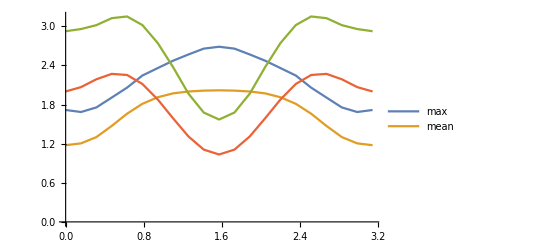

```mathematica
ListLinePlot[{wrsnmax,wrsnmean,rdnmax,rdmean},PlotLegends->{"max","mean"}]
```

```mathematica
ListLinePlot[Table[fibon[[n]],{n,1,6}]]
```

Part::partd: Part specification fibon⟦1⟧ is longer than depth of object.

Part::partd: Part specification fibon⟦2⟧ is longer than depth of object.

Part::partd: Part specification fibon⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

## dt = pi/8 kick*after

#### data

```mathematica
w8rsdata={-0.000000000000000000*10^+00,1.201752073385713215*10^+00,1.404764034988925214*10^+00,2.233645517748446441*10^+00,1.404764034988925658*10^+00,1.624883029461677619*10^+00,2.278389197645120046*10^+00,1.624883029461678285*10^+00,1.593851164854307223*10^+00,8.216731072033635064*10^-01,1.290544393841768223*10^+00,2.089530831627514740*10^+00,3.325385017234641527*10^+00,3.523440540975488755*10^+00,2.668568627582057040*10^+00,3.523440540975493640*10^+00,2.668568627582057484*10^+00,2.351196826909814241*10^+00,2.318686453377657219*10^+00,1.593851164854319435*10^+00,2.318686453377660772*10^+00,2.776169630642704611*10^+00,2.804050511744111240*10^+00,2.776169630642706387*10^+00,2.804050511744112129*10^+00,2.299445460700329846*10^+00,1.930650986025548299*10^+00,1.898089215623047110*10^+00,2.494922218926647339*10^+00,2.163343845725249182*10^+00,2.351196826909824455*10^+00,2.163343845725250514*10^+00,1.707585496495206190*10^+00,1.576026656233676881*10^+00,1.864582378506179028*10^+00,2.195885753545303132*10^+00,1.864582378506178584*10^+00,2.190551101783464016*10^+00,2.860620877607966683*10^+00,2.190551101783464460*10^+00,2.224250692552391495*10^+00,2.422856941345244763*10^+00,2.167641295114398847*10^+00,2.334902662302655418*10^+00,2.520491968165093688*10^+00,2.711302851583177631*10^+00,2.748362538649646858*10^+00,2.711302851583176743*10^+00,2.433012581815443998*10^+00,1.691154049940058801*10^+00,2.230474635103977477*10^+00,1.596161745402707055*10^+00,2.230474635103978365*10^+00,2.645887833122746891*10^+00,3.456553679528867384*10^+00,2.645887833122746891*10^+00,3.456553679528869605*10^+00,2.584704531161082564*10^+00,2.345132247606239950*10^+00,1.701238850520315982*10^+00,2.137775380373765799*10^+00,1.355782456921178714*10^+00,1.691154049940056359*10^+00,1.355782456921181156*10^+00,1.691154049940056137*10^+00,2.230474635103977921*10^+00,2.645887833122750443*10^+00,3.456553679528884260*10^+00,2.645887833122751331*10^+00,2.542573442343517343*10^+00,2.579213494286423547*10^+00,2.542573442343518231*10^+00,2.200234818693169281*10^+00,2.712920251850555964*10^+00,2.620049674028311237*10^+00,3.036822097722390090*10^+00,2.266390890715524797*10^+00,2.310805005455661920*10^+00,1.519211695330241030*10^+00,2.310805005455663697*10^+00,1.519211695330242584*10^+00,1.757304231762748969*10^+00,1.220858135955107171*10^+00,2.200234818693176386*10^+00,1.220858135955109169*10^+00,3.347850980164042700*10^-01,1.337654412153505223*10^+00,3.347850980164008838*10^-01,1.337654412153507000*10^+00,2.190054603804616473*10^+00,2.070248918711005359*10^+00,2.509889490403449663*10^+00,2.084693479056893839*10^+00,2.289564666248968816*10^+00,1.757304231762767177*10^+00,2.289564666248969704*10^+00,1.757304231762767177*10^+00,1.220858135955107615*10^+00,3.347850980163983303*10^-01,1.337654412153505223*10^+00,3.347850980163979973*10^-01,1.214578201164809190*10^+00,1.996346694004163425*10^+00,1.214578201164808968*10^+00,9.025331750545201315*10^-01,1.545388365334364078*10^+00,1.797423787115928207*10^+00,2.481456449173589540*10^+00,2.745638527433412968*10^+00,2.425460185211854025*10^+00,3.208249356211450465*10^+00,2.425460185211854469*10^+00,1.836145751145073612*10^+00,2.436391693696628113*10^+00,2.769109278959754228*10^+00,3.405051551091419881*10^+00,2.769109278959757781*10^+00,2.529135051241345522*10^+00,2.480391579015364112*10^+00,2.529135051241346854*10^+00,2.480391579015362780*10^+00,1.849079092681482850*10^+00,1.644068909671546619*10^+00,1.178637710265606930*10^+00,1.246702955486297615*10^+00,1.967957155928254487*10^+00,2.436391693696637439*10^+00,1.967957155928256929*10^+00,1.407085065959675418*10^+00,1.684869631617548880*10^+00,1.081566411385610937*10^+00,1.791484430865424526*10^+00,1.081566411385611159*10^+00,1.445948341811814197*10^+00,2.254516899127482432*10^+00,1.445948341811814863*10^+00,1.420309952716547919*10^+00,1.013309432378542319*10^+00,1.679226740023570086*10^+00,2.272513795934354874*10^+00,2.779735438914158863*10^+00,2.732840440064581600*10^+00,2.067437688110914440*10^+00,2.732840440064583820*10^+00,2.067437688110914884*10^+00,1.872926929026522469*10^+00,1.849364975949924217*10^+00,1.420309952716558799*10^+00,1.849364975949923551*10^+00,2.076739681945461324*10^+00,2.546534747055225534*10^+00,2.076739681945461324*10^+00,2.546534747055224646*10^+00,2.809279149305390355*10^+00,2.800090058034910179*10^+00,2.812831525511446884*10^+00,2.567218809214985242*10^+00,2.433211397748682003*10^+00,1.872926929026520693*10^+00,2.433211397748681115*10^+00,2.100951255295684383*10^+00,1.724055648888458636*10^+00,2.139530859034457944*10^+00,1.361358620108681361*10^+00,2.139530859034457499*10^+00,2.973009283288681637*10^+00,3.557076402054127229*10^+00,2.973009283288682969*10^+00,3.197623160978526169*10^+00,2.321149556090520427*10^+00,2.289431197674496321*10^+00,1.644613891109840909*10^+00,1.954159808260681253*10^+00,1.375441508118774747*10^+00,1.930524678881335054*10^+00,1.375441508118773415*10^+00,1.186873143321225621*10^+00,1.394602973947438818*10^+00,1.242682655104635048*10^+00,1.742893180631943650*10^+00,1.242682655104635492*10^+00,1.610007776631110499*10^+00,2.454000293633377794*10^+00,1.610007776631110721*10^+00,2.454000293633378682*10^+00,3.011563542036870711*10^+00,2.719365321693308246*10^+00,1.998896957465066127*10^+00,1.592193194484436747*10^+00,1.815439570121786028*10^+00,1.394602973947435487*10^+00,1.815439570121786694*10^+00,2.217473099908383372*10^+00,2.605562665538264877*10^+00,2.119675102813395995*10^+00,1.589326185822854454*10^+00,2.119675102813399103*10^+00,2.483785293152564577*10^+00,2.586046702436786138*10^+00,2.483785293152564577*10^+00,2.722912528242654327*10^-14,1.201752073385712993*10^+00,1.404881290126556603*10^+00,2.217273218841613769*10^+00,1.404881290126559268*10^+00,1.618334329357092427*10^+00,2.240807294759564972*10^+00,1.618334329357092649*10^+00,1.645520976853169337*10^+00,9.378152660583737310*10^-01,1.374841989669165265*10^+00,2.134032730713412818*10^+00,3.264803814773208135*10^+00,3.463468598210527549*10^+00,2.692986557954549554*10^+00,3.463468598210531546*10^+00,2.692986557954550442*10^+00,2.394123488654254839*10^+00,2.339685188497897528*10^+00,1.690132005226524070*10^+00,2.339685188497899748*10^+00,2.758468515340537941*10^+00,2.755147642250962647*10^+00,2.758468515340538829*10^+00,2.755147642250962203*10^+00,2.335352967284020753*10^+00,1.966778325469036304*10^+00,1.979632243950241843*10^+00,2.513796580776619827*10^+00,2.235722729295053224*10^+00,2.427543850808992598*10^+00,2.235722729295053224*10^+00,1.863577384938605253*10^+00,1.673754381818773451*10^+00,1.939634745964421203*10^+00,2.283684839760725893*10^+00,1.939634745964421203*10^+00,2.254085543346625364*10^+00,2.896181497872664323*10^+00,2.254085543346625364*10^+00,2.292692386764148438*10^+00,2.535426481375661734*10^+00,2.320987483465496659*10^+00,2.467496568754325992*10^+00,2.566773449317167888*10^+00,2.727459155496130272*10^+00,2.720432814978809954*10^+00,2.727459155496131160*10^+00,2.463275293358052398*10^+00,1.780401878705387242*10^+00,2.271656107093216193*10^+00,1.627174067328053697*10^+00,2.271656107093217081*10^+00,2.682746657696794212*10^+00,3.432517858924107212*10^+00,2.682746657696793768*10^+00,3.432517858924109433*10^+00,2.695249798005530106*10^+00,2.518202193442008241*10^+00,1.987436405822265106*10^+00,2.356136663042097013*10^+00,1.639922086651709021*10^+00,1.877236200708722880*10^+00,1.639922086651710575*10^+00,1.877236200708721547*10^+00,2.309884808812504797*10^+00,2.676704549390691579*10^+00,3.381982161243981988*10^+00,2.676704549390693799*10^+00,2.600072541476596832*10^+00,2.644437528069199850*10^+00,2.600072541476597721*10^+00,2.256687876705123941*10^+00,2.698950235036034151*10^+00,2.615207306507349561*10^+00,2.992753807675427424*10^+00,2.303017530476431762*10^+00,2.355497513454549274*10^+00,1.660203371454533672*10^+00,2.355497513454550607*10^+00,1.660203371454537002*10^+00,1.906239012316955250*10^+00,1.363897056903055738*10^+00,2.213131674452533115*10^+00,1.363897056903058402*10^+00,5.762863807945340922*10^-01,1.501189437130702409*10^+00,5.762863807945335370*10^-01,1.501189437130703963*10^+00,2.305901977709882367*10^+00,2.117966616237542787*10^+00,2.479480203101330549*10^+00,2.066004314216018045*10^+00,2.238487614179265339*10^+00,1.743289898225418355*10^+00,2.238487614179264451*10^+00,1.743289898225418133*10^+00,1.228818281980796234*10^+00,3.146218988534248973*10^-01,1.325507196206429317*10^+00,3.146218988534243421*10^-01,1.193940401791551587*10^+00,1.935733832951682665*10^+00,1.193940401791551809*10^+00,9.127536626191535829*10^-01,1.550913206326928862*10^+00,1.810176007510659657*10^+00,2.481804751550895194*10^+00,2.745655055659728561*10^+00,2.438401124296956546*10^+00,3.159312118893250698*10^+00,2.438401124296957434*10^+00,1.961354012752293485*10^+00,2.521055430576278233*10^+00,2.755172862960182822*10^+00,3.331668656714763976*10^+00,2.755172862960183267*10^+00,2.554115123909793006*10^+00,2.444845351204398831*10^+00,2.554115123909792562*10^+00,2.444845351204399275*10^+00,1.899787353637255594*10^+00,1.710690728365649171*10^+00,1.340570648991996183*10^+00,1.367455861044706733*10^+00,2.030331800109445251*10^+00,2.449509785221870573*10^+00,2.030331800109449247*10^+00,1.543906679185949482*10^+00,1.788631683075762924*10^+00,1.214454778948544922*10^+00,1.864201097323985312*10^+00,1.214454778948544034*10^+00,1.552644544352221878*10^+00,2.299877725773910253*10^+00,1.552644544352223654*10^+00,1.534808110560652361*10^+00,1.239336794577865053*10^+00,1.873156995782023326*10^+00,2.379050527245555102*10^+00,2.749248744322287941*10^+00,2.698339595417642123*10^+00,2.046063123020462005*10^+00,2.698339595417644343*10^+00,2.046063123020460228*10^+00,1.908034440911858365*10^+00,1.865975306520649912*10^+00,1.512797864341550946*10^+00,1.865975306520648358*10^+00,2.044996545035305591*10^+00,2.516809437968989371*10^+00,2.044996545035304258*10^+00,2.516809437968988927*10^+00,2.790481537534977186*10^+00,2.807691838243843385*10^+00,2.875743950136464999*10^+00,2.636979480206376181*10^+00,2.498024762075573335*10^+00,1.964331658414465220*10^+00,2.498024762075573335*10^+00,2.211078288386741697*10^+00,1.919378435812347794*10^+00,2.243623891927045033*10^+00,1.497170988526309587*10^+00,2.243623891927047254*10^+00,2.999367519251859626*10^+00,3.524340463575388327*10^+00,2.999367519251861847*10^+00,3.183095588883420035*10^+00,2.320940192214536957*10^+00,2.294111359867350597*10^+00,1.632344455711174813*10^+00,1.929915580179820012*10^+00,1.398738082010620998*10^+00,1.956946184157585922*10^+00,1.398738082010620998*10^+00,1.220161603151123542*10^+00,1.436642677171796167*10^+00,1.203544548189235952*10^+00,1.747435437885037857*10^+00,1.203544548189236618*10^+00,1.606046970777451399*10^+00,2.445533842378319278*10^+00,1.606046970777450511*10^+00,2.445533842378319722*10^+00,3.009802708865650267*10^+00,2.753598930168538850*10^+00,2.095428973237255299*10^+00,1.692622567988003368*10^+00,1.854947444627202291*10^+00,1.428111202468843155*10^+00,1.854947444627203179*10^+00,2.223846520527024584*10^+00,2.593363902347296523*10^+00,2.135263452843718213*10^+00,1.642176324444931002*10^+00,2.135263452843720877*10^+00,2.480077108690629029*10^+00,2.555397797291843798*10^+00,2.480077108690629473*10^+00,-9.610279511444755881*10^-16,1.201752073385714326*10^+00,1.406549003615073845*10^+00,2.171656847108323518*10^+00,1.406549003615075177*10^+00,1.607378642142087255*10^+00,2.144042017716827786*10^+00,1.607378642142089031*10^+00,1.764401103105462942*10^+00,1.153545603088931948*10^+00,1.473534182783539759*10^+00,2.211272218508021581*10^+00,3.087164324994342124*10^+00,3.298753378244593915*10^+00,2.769404146823792878*10^+00,3.298753378244595247*10^+00,2.769404146823794211*10^+00,2.548862918633272301*10^+00,2.414854455307543279*10^+00,1.935570248557540562*10^+00,2.414854455307543724*10^+00,2.709209421708954402*10^+00,2.630839034475554783*10^+00,2.709209421708955290*10^+00,2.630839034475556115*10^+00,2.358705656385536198*10^+00,2.008763381884320243*10^+00,2.081832775465084495*10^+00,2.532410624317977366*10^+00,2.402230609139417439*10^+00,2.616330528958225710*10^+00,2.402230609139417439*10^+00,2.081663193772020470*10^+00,1.861676245324804135*10^+00,2.079914348747903041*10^+00,2.454520637086418766*10^+00,2.079914348747903041*10^+00,2.360196240499348619*10^+00,2.919675521374951899*10^+00,2.360196240499348175*10^+00,2.406803828185924310*10^+00,2.727590738767923462*10^+00,2.595977061444075140*10^+00,2.692299799500867952*10^+00,2.608666634939901030*10^+00,2.692362048317725964*10^+00,2.624692678282997349*10^+00,2.692362048317728185*10^+00,2.500572916295619841*10^+00,1.965018607150226471*10^+00,2.364438899753672718*10^+00,1.698008780067070012*10^+00,2.364438899753674050*10^+00,2.722555621287046979*10^+00,3.344902678389529260*10^+00,2.722555621287048311*10^+00,3.344902678389529704*10^+00,2.896699879561561275*10^+00,2.754417088148864323*10^+00,2.451117270924966007*10^+00,2.759451579147460087*10^+00,2.185242465737216921*10^+00,2.228138438644170272*10^+00,2.185242465737217366*10^+00,2.228138438644170272*10^+00,2.455518944295232764*10^+00,2.733927376536085418*10^+00,3.202517687832254545*10^+00,2.733927376536085863*10^+00,2.706716014642617019*10^+00,2.783218971225229765*10^+00,2.706716014642617463*10^+00,2.392867194626030702*10^+00,2.666427784059155037*10^+00,2.613818821852629704*10^+00,2.891280479703016049*10^+00,2.405676394005860530*10^+00,2.455735490219932871*10^+00,1.975090897533118728*10^+00,2.455735490219934203*10^+00,1.975090897533120726*10^+00,2.159918974360121258*10^+00,1.646355874715887513*10^+00,2.219073419965954308*10^+00,1.646355874715889067*10^+00,1.080780515297598887*10^+00,1.884123891631425352*10^+00,1.080780515297598665*10^+00,1.884123891631426684*10^+00,2.516206302771199166*10^+00,2.254278447278883490*10^+00,2.411762678681284910*10^+00,2.059893051503939088*10^+00,2.148762595887910187*10^+00,1.726233231181890204*10^+00,2.148762595887910631*10^+00,1.726233231181889538*10^+00,1.314496450705311847*10^+00,3.517847211888392445*10^-01,1.365075771189549370*10^+00,3.517847211888386894*10^-01,1.149054473611351490*10^+00,1.776853981682442019*10^+00,1.149054473611352156*10^+00,9.912095781899419311*10^-01,1.611129655334017752*10^+00,1.871440950928522140*10^+00,2.501749777648908157*10^+00,2.729733488509006989*10^+00,2.405931649649308834*10^+00,2.977425085827461348*10^+00,2.405931649649309723*10^+00,2.190910718289267756*10^+00,2.694694615659384507*10^+00,2.705273000892159274*10^+00,3.137963372385750738*10^+00,2.705273000892159274*10^+00,2.580976630643827097*10^+00,2.330246400380991734*10^+00,2.580976630643827541*10^+00,2.330246400380991734*10^+00,1.925927702526272212*10^+00,1.767627398161096375*10^+00,1.616367501627038017*10^+00,1.624368431771276322*10^+00,2.200954341510645840*10^+00,2.482435412968321042*10^+00,2.200954341510649392*10^+00,1.862346693249737672*10^+00,2.004267118561045891*10^+00,1.551586009166050717*10^+00,2.080871410876645289*10^+00,1.551586009166051161*10^+00,1.785364722481902700*10^+00,2.385304317425272380*10^+00,1.785364722481904032*10^+00,1.753083045170627630*10^+00,1.716857849991029195*10^+00,2.248978180694519935*10^+00,2.574100148007209210*10^+00,2.684000901051970978*10^+00,2.641854507285050335*10^+00,2.012820142760989750*10^+00,2.641854507285053444*10^+00,2.012820142760989306*10^+00,2.006087233367333411*10^+00,1.903962534977175824*10^+00,1.785316064367709510*10^+00,1.903962534977176047*10^+00,1.979199342371316561*10^+00,2.441969664050978928*10^+00,1.979199342371317671*10^+00,2.441969664050980260*10^+00,2.769247600854493285*10^+00,2.825733504740014723*10^+00,2.963024065440392096*10^+00,2.691001568990635473*10^+00,2.562332211239420232*10^+00,2.057408567944672306*10^+00,2.562332211239422008*10^+00,2.384192067421603944*10^+00,2.277668949558377065*10^+00,2.412877224208775484*10^+00,1.783254330320277470*10^+00,2.412877224208775484*10^+00,3.024695969734315426*10^+00,3.393795275633404884*10^+00,3.024695969734315426*10^+00,3.107940291917094644*10^+00,2.289588472224528992*10^+00,2.293935117584387395*10^+00,1.609345061004137545*10^+00,1.845052400418572880*10^+00,1.446794888457205719*10^+00,2.027851938750854899*10^+00,1.446794888457206829*10^+00,1.289658426809482394*10^+00,1.458864319272782595*10^+00,1.090821753368750757*10^+00,1.745103601884227196*10^+00,1.090821753368750313*10^+00,1.578794741566082571*10^+00,2.402053447666009589*10^+00,1.578794741566082793*10^+00,2.402053447666010033*10^+00,3.008456043616004827*10^+00,2.806565909367844558*10^+00,2.287704458575930744*10^+00,1.867166239589882704*10^+00,1.956906460667953596*10^+00,1.460004962873191925*10^+00,1.956906460667955372*10^+00,2.239067083037546535*10^+00,2.552238470079166710*10^+00,2.178298417417310784*10^+00,1.765763127882223671*10^+00,2.178298417417313892*10^+00,2.486421777966441482*10^+00,2.482310239090645521*10^+00,2.486421777966442370*10^+00,9.610279511444749964*10^-16,1.201752073385713659*10^+00,1.413071973816222071*10^+00,2.117344506457177644*10^+00,1.413071973816223625*10^+00,1.624417752822836958*10^+00,2.029545287444445290*10^+00,1.624417752822837624*10^+00,1.900682337109401043*10^+00,1.410136432185759459*10^+00,1.564338917123458295*10^+00,2.229242440389795465*10^+00,2.841871607282506318*10^+00,3.089899643874818302*10^+00,2.838374022621964254*10^+00,3.089899643874821411*10^+00,2.838374022621962922*10^+00,2.737766260598769819*10^+00,2.546006244717883504*10^+00,2.218904897672426824*10^+00,2.546006244717883504*10^+00,2.670755311506200158*10^+00,2.477606001800494173*10^+00,2.670755311506201046*10^+00,2.477606001800495061*10^+00,2.309825521747523425*10^+00,1.975909015539287772*10^+00,2.122602450163194376*10^+00,2.510515997297716240*10^+00,2.521211659437896380*10^+00,2.834067426006906754*10^+00,2.521211659437895936*10^+00,2.223318815612201682*10^+00,2.006853491437648351*10^+00,2.175313524332600945*10^+00,2.606962347413172676*10^+00,2.175313524332600945*10^+00,2.374835812743603114*10^+00,2.814491599373575070*10^+00,2.374835812743602670*10^+00,2.438656707876385887*10^+00,2.838175827009357555*10^+00,2.773444649416399344*10^+00,2.809456450650475112*10^+00,2.564307881840130143*10^+00,2.583498507540672229*10^+00,2.451608557829036528*10^+00,2.583498507540673117*10^+00,2.423804971305563605*10^+00,2.082632555579136291*10^+00,2.399208657795761646*10^+00,1.778607144800366857*10^+00,2.399208657795763422*10^+00,2.704760921481770275*10^+00,3.186636066890225827*10^+00,2.704760921481772940*10^+00,3.186636066890228491*10^+00,3.008082811427794656*10^+00,2.864961378517006274*10^+00,2.803750761711134132*10^+00,3.067955642815442197*10^+00,2.657932101961950622*10^+00,2.517549426360448983*10^+00,2.657932101961952398*10^+00,2.517549426360448983*10^+00,2.547519057356474548*10^+00,2.771411275577571054*10^+00,3.000480893317703845*10^+00,2.771411275577571942*10^+00,2.818843494311087827*10^+00,2.911056978379908511*10^+00,2.818843494311088715*10^+00,2.554363556286874726*10^+00,2.674991328193635276*10^+00,2.642894244448075636*10^+00,2.819064422159304861*10^+00,2.530491160608678403*10^+00,2.536053512987536784*10^+00,2.199326395104193033*10^+00,2.536053512987538561*10^+00,2.199326395104196141*10^+00,2.299103395331910438*10^+00,1.895219010389754377*10^+00,2.239752191709578177*10^+00,1.895219010389755487*10^+00,1.577770081750413667*10^+00,2.260547471005069031*10^+00,1.577770081750415221*10^+00,2.260547471005071252*10^+00,2.677909550602726618*10^+00,2.416611763668243817*10^+00,2.434670330399298255*10^+00,2.185976836925751954*10^+00,2.126220427491759324*10^+00,1.798058802325512184*10^+00,2.126220427491758880*10^+00,1.798058802325512184*10^+00,1.526964494826955843*10^+00,6.036529687469083250*10^-01,1.554524614053660825*10^+00,6.036529687469078809*10^-01,1.236996503653904567*10^+00,1.728627165872560933*10^+00,1.236996503653905011*10^+00,1.161769705442457834*10^+00,1.817330473282377623*10^+00,2.017499142369317155*10^+00,2.565182186911205253*10^+00,2.658199562142259609*10^+00,2.311042815156364671*10^+00,2.629545991512898695*10^+00,2.311042815156366004*10^+00,2.370374261797305149*10^+00,2.807468947281171801*10^+00,2.604476130095457975*10^+00,2.871601181835321981*10^+00,2.604476130095458863*10^+00,2.565569814143020544*10^+00,2.153403747336879892*10^+00,2.565569814143020988*10^+00,2.153403747336879892*10^+00,1.875236965013860724*10^+00,1.719176945587927552*10^+00,1.856441395948183803*10^+00,1.848901736964409181*10^+00,2.346679093812023886*10^+00,2.534134244288194004*10^+00,2.346679093812027439*10^+00,2.140816035260985295*10^+00,2.212105295100486035*10^+00,1.879239732014128306*10^+00,2.348744426298340571*10^+00,1.879239732014125641*10^+00,2.015501039757837010*10^+00,2.436563255410145512*10^+00,2.015501039757840118*10^+00,1.974597770909274796*10^+00,2.156952246129531403*10^+00,2.599750695412017532*10^+00,2.721790623584951163*10^+00,2.587193632068018445*10^+00,2.548337092771592260*10^+00,1.985043682198511128*10^+00,2.548337092771594037*10^+00,1.985043682198511572*10^+00,2.084704976521846831*10^+00,1.930903053734947639*10^+00,2.077339314687402627*10^+00,1.930903053734946084*10^+00,1.931673931035102765*10^+00,2.388950161904157987*10^+00,1.931673931035102543*10^+00,2.388950161904159764*10^+00,2.766002756072526658*10^+00,2.817237497761484910*10^+00,3.013979389716061164*10^+00,2.646303989389015676*10^+00,2.488362613714926841*10^+00,2.018970438334809714*10^+00,2.488362613714927729*10^+00,2.471872831064371390*10^+00,2.589124287903246113*10^+00,2.502945432185085917*10^+00,2.029982218163191465*10^+00,2.502945432185085917*10^+00,2.994948159523660891*10^+00,3.161744548970920832*10^+00,2.994948159523662223*10^+00,2.964490438355293467*10^+00,2.245685622068086307*10^+00,2.282986625728595342*10^+00,1.567337888754102737*10^+00,1.728018976373781657*10^+00,1.560481576946356919*10^+00,2.154226728648075184*10^+00,1.560481576946357141*10^+00,1.425685496502195893*10^+00,1.480860305321390680*10^+00,9.681389039352626957*10^-01,1.679493500377966964*10^+00,9.681389039352628068*10^-01,1.579071594942197176*10^+00,2.343393971594130765*10^+00,1.579071594942196510*10^+00,2.343393971594131653*10^+00,3.017691746299051125*10^+00,2.820954134504105593*10^+00,2.412513745219281081*10^+00,2.004487832954583659*10^+00,2.032923040079711363*10^+00,1.480433408371804926*10^+00,2.032923040079711363*10^+00,2.275935827443400505*10^+00,2.486473032252554560*10^+00,2.236857199116023320*10^+00,1.865549213611780166*10^+00,2.236857199116026429*10^+00,2.526323189704774208*10^+00,2.465174770533302251*10^+00,2.526323189704775984*10^+00,4.805139755722374982*10^-16,1.201752073385713881*10^+00,1.428059645285720158*10^+00,2.048374937697135856*10^+00,1.428059645285721935*10^+00,1.666480003267421406*10^+00,1.936669214298421871*10^+00,1.666480003267423626*10^+00,2.052740825892120036*10^+00,1.643080743007856448*10^+00,1.661812934626155425*10^+00,2.224860856919438579*10^+00,2.654050610985168035*10^+00,2.962636566775188829*10^+00,2.907044499855478303*10^+00,2.962636566775189273*10^+00,2.907044499855477859*10^+00,2.924827604171466255*10^+00,2.716473234210650567*10^+00,2.512068315142141905*10^+00,2.716473234210650567*10^+00,2.655934538218130747*10^+00,2.317311272882546014*10^+00,2.655934538218131191*10^+00,2.317311272882546902*10^+00,2.220307464479274628*10^+00,2.012191726856501717*10^+00,2.179992416253241583*10^+00,2.499903823976390438*10^+00,2.561402880273283333*10^+00,2.937554494924645265*10^+00,2.561402880273283333*10^+00,2.266573685517698333*10^+00,2.127419876375568286*10^+00,2.164694334337399440*10^+00,2.671520648075005777*10^+00,2.164694334337401216*10^+00,2.289955671785683489*10^+00,2.553784108780871698*10^+00,2.289955671785683933*10^+00,2.426861344095669892*10^+00,2.830695883441989746*10^+00,2.780240756788796119*10^+00,2.783768961913103190*10^+00,2.403502009787139126*10^+00,2.431748107300392370*10^+00,2.243788282073493345*10^+00,2.431748107300394590*10^+00,2.258660208031495920*10^+00,2.085841896820527896*10^+00,2.360178683752486073*10^+00,1.871425451148097885*10^+00,2.360178683752487405*10^+00,2.603634438826492037*10^+00,2.994119018538764276*10^+00,2.603634438826492925*10^+00,2.994119018538764276*10^+00,3.005325990796015034*10^+00,2.837019592317211014*10^+00,2.951687222296734525*10^+00,3.187333447996583136*10^+00,2.919643142084341836*10^+00,2.681540428891030725*10^+00,2.919643142084342724*10^+00,2.681540428891030725*10^+00,2.536230128985066390*10^+00,2.790873981414659699*10^+00,2.816964511884369582*10^+00,2.790873981414660587*10^+00,2.895888049117939289*10^+00,2.983680264897899281*10^+00,2.895888049117940177*10^+00,2.708926359770259751*10^+00,2.680165184960537683*10^+00,2.692840073962402769*10^+00,2.772058881912546902*10^+00,2.607099999539660207*10^+00,2.540905735455471159*10^+00,2.266535429128951673*10^+00,2.540905735455471159*10^+00,2.266535429128953893*10^+00,2.294559165738335960*10^+00,2.056677179378370912*10^+00,2.280825597761409362*10^+00,2.056677179378372244*10^+00,1.953472660170663122*10^+00,2.525667871692552247*10^+00,1.953472660170664010*10^+00,2.525667871692554023*10^+00,2.741238104724306179*10^+00,2.536262147835722125*10^+00,2.475126442828633699*10^+00,2.380744988840377552*10^+00,2.200861445653917947*10^+00,1.938620522520004830*10^+00,2.200861445653918391*10^+00,1.938620522520005274*10^+00,1.787086763788324539*10^+00,1.034745087459607582*10^+00,1.828135104321573667*10^+00,1.034745087459605806*10^+00,1.487518889417676515*10^+00,1.817259808728220127*10^+00,1.487518889417676959*10^+00,1.427780261019934382*10^+00,2.113771765715624085*10^+00,2.245077983674131694*10^+00,2.649437120216531660*10^+00,2.533237842207804569*10^+00,2.201973716145604332*10^+00,2.229875649248913128*10^+00,2.201973716145606108*10^+00,2.484819706258567962*10^+00,2.831446438408482535*10^+00,2.460706852570706094*10^+00,2.590824545602893103*10^+00,2.460706852570704761*10^+00,2.577573558770549056*10^+00,2.036792796381910353*10^+00,2.577573558770549944*10^+00,2.036792796381910353*10^+00,1.800868555786897529*10^+00,1.687196863509330624*10^+00,1.971273448108884274*10^+00,1.980283485128456755*10^+00,2.407836572226899730*10^+00,2.570167796474128075*10^+00,2.407836572226902838*10^+00,2.299775179480566756*10^+00,2.340268250430727281*10^+00,2.124307568245513700*10^+00,2.543657399289867005*10^+00,2.124307568245512368*10^+00,2.175746419687674127*10^+00,2.459208912415210779*10^+00,2.175746419687677680*10^+00,2.117922120484975412*10^+00,2.402858218641774180*10^+00,2.775470715643398201*10^+00,2.704089674374016372*10^+00,2.449209282770902885*10^+00,2.441910417486727880*10^+00,1.969141889147833169*10^+00,2.441910417486729656*10^+00,1.969141889147833613*10^+00,2.138775546704677399*10^+00,2.017449536231232354*10^+00,2.314500084406371894*10^+00,2.017449536231231910*10^+00,1.919565349965591805*10^+00,2.391154082898543365*10^+00,1.919565349965592249*10^+00,2.391154082898545141*10^+00,2.788615738174220038*10^+00,2.779076857993322935*10^+00,3.012049163675183383*10^+00,2.548075495923689981*10^+00,2.326400584927954096*10^+00,1.904524611078011631*10^+00,2.326400584927953652*10^+00,2.426038552445537011*10^+00,2.740230429091752296*10^+00,2.543686857635329979*10^+00,2.257576993126198861*10^+00,2.543686857635329090*10^+00,2.948636168343493846*10^+00,2.922324179110688203*10^+00,2.948636168343495179*10^+00,2.832239564660374409*10^+00,2.285051455488745553*10^+00,2.326383536406726904*10^+00,1.667594479959980447*10^+00,1.673531741521668614*10^+00,1.810711147873215410*10^+00,2.347948295432590093*10^+00,1.810711147873216742*10^+00,1.688146652117477720*10^+00,1.542471411052538599*10^+00,1.017953351963138298*10^+00,1.661718673688853842*10^+00,1.017953351963138520*10^+00,1.676220039548275142*10^+00,2.348859241851630308*10^+00,1.676220039548273810*10^+00,2.348859241851630753*10^+00,3.003996029953254876*10^+00,2.853856362699609850*10^+00,2.481730314580683494*10^+00,2.071989993380114470*10^+00,2.064808384652855988*10^+00,1.516941240335488050*10^+00,2.064808384652857765*10^+00,2.289614902098351390*10^+00,2.451487626005218967*10^+00,2.281657006362930673*10^+00,1.944589649570451773*10^+00,2.281657006362933338*10^+00,2.572364295123315880*10^+00,2.476379526146317733*10^+00,2.572364295123315880*10^+00,3.203426503814917641*10^-16,1.201752073385713659*10^+00,1.453383295463395397*10^+00,1.986421649466675321*10^+00,1.453383295463396285*10^+00,1.748614537443929917*10^+00,1.916475494221603348*10^+00,1.748614537443931916*10^+00,2.221389124509349777*10^+00,1.837127007711991666*10^+00,1.757349002284554595*10^+00,2.239489442481733761*10^+00,2.583379781160932698*10^+00,2.899269622969394611*10^+00,2.976579552930860295*10^+00,2.899269622969395055*10^+00,2.976579552930858963*10^+00,3.086645603688424444*10^+00,2.845141753394230921*10^+00,2.713544155468990304*10^+00,2.845141753394232698*10^+00,2.639974738587843373*10^+00,2.208441569192208132*10^+00,2.639974738587843817*10^+00,2.208441569192209020*10^+00,2.137744243144623191*10^+00,2.131876509802306252*10^+00,2.277536127246362341*10^+00,2.558640119223468457*10^+00,2.529998312282983441*10^+00,2.861487806145244672*10^+00,2.529998312282983886*10^+00,2.328807459143590997*10^+00,2.261354551112720657*10^+00,2.118956344501606193*10^+00,2.657781861025184433*10^+00,2.118956344501605749*10^+00,2.184675108946975364*10^+00,2.232315082587619237*10^+00,2.184675108946976252*10^+00,2.444943483197191014*10^+00,2.770424428770803971*10^+00,2.705085488072866529*10^+00,2.678126017880098964*10^+00,2.224636681982248287*10^+00,2.273601359060359428*10^+00,2.087713116815125947*10^+00,2.273601359060361204*10^+00,2.093306214169295743*10^+00,2.014934209823030287*10^+00,2.303113121177935430*10^+00,1.976223939794389484*10^+00,2.303113121177935430*10^+00,2.492006894894531754*10^+00,2.813325562172828143*10^+00,2.492006894894531754*10^+00,2.813325562172829031*10^+00,2.921791004489815435*10^+00,2.743563110499406044*10^+00,2.944853000637418283*10^+00,3.149388261532511279*10^+00,2.968973112657062874*10^+00,2.698687175338770672*10^+00,2.968973112657063762*10^+00,2.698687175338770672*10^+00,2.531993904704063603*10^+00,2.761140689908842205*10^+00,2.654377571785036860*10^+00,2.761140689908843537*10^+00,2.929830253820278951*10^+00,2.996504991083201119*10^+00,2.929830253820279840*10^+00,2.841121877206687074*10^+00,2.682710924645868467*10^+00,2.720897394057164576*10^+00,2.755919810997916830*10^+00,2.592273901029180649*10^+00,2.465037596389944241*10^+00,2.214637144174392169*10^+00,2.465037596389944685*10^+00,2.214637144174393946*10^+00,2.218200327432420238*10^+00,2.161992037575330539*10^+00,2.370445827852753151*10^+00,2.161992037575331427*10^+00,2.151986905732225175*10^+00,2.608297233401450921*10^+00,2.151986905732226063*10^+00,2.608297233401453585*10^+00,2.713915398140993140*10^+00,2.587915745935072565*10^+00,2.489907548456969710*10^+00,2.519620031368857038*10^+00,2.275381686137122550*10^+00,2.085688283799225662*10^+00,2.275381686137121662*10^+00,2.085688283799225662*10^+00,2.077988847477270529*10^+00,1.534866128739493352*10^+00,2.157054049561726750*10^+00,1.534866128739492463*10^+00,1.861514972794711120*10^+00,1.998189485491503881*10^+00,1.861514972794713563*10^+00,1.767395373672909109*10^+00,2.400907965744354833*10^+00,2.466955358296528900*10^+00,2.713230607356936552*10^+00,2.444607383811105095*10^+00,2.191849613158872945*10^+00,1.950167182366527197*10^+00,2.191849613158874277*10^+00,2.537015067013194347*10^+00,2.780629327809433171*10^+00,2.347947351337039912*10^+00,2.361752164350526151*10^+00,2.347947351337039024*10^+00,2.624408959312561240*10^+00,2.044681954595022333*10^+00,2.624408959312560352*10^+00,2.044681954595022777*10^+00,1.817900498044652036*10^+00,1.804625439925199526*10^+00,2.016250355863926647*10^+00,2.024186825225655184*10^+00,2.397168763193518792*10^+00,2.541957291825225340*10^+00,2.397168763193521457*10^+00,2.370148130700449496*10^+00,2.336787398727232734*10^+00,2.219874059126750510*10^+00,2.595525376655857031*10^+00,2.219874059126750510*10^+00,2.259641016514567724*10^+00,2.485259534501819356*10^+00,2.259641016514569944*10^+00,2.201927983490388652*10^+00,2.419191359545197262*10^+00,2.730885435101876091*10^+00,2.523443515219210731*10^+00,2.320188362214949951*10^+00,2.338804551686723965*10^+00,1.993758295876365105*10^+00,2.338804551686725297*10^+00,1.993758295876364883*10^+00,2.227037358981643678*10^+00,2.161870351441693927*10^+00,2.500307505220243254*10^+00,2.161870351441694815*10^+00,1.996920988701086142*10^+00,2.484084472101211638*10^+00,1.996920988701087030*10^+00,2.484084472101212970*10^+00,2.799653636858132622*10^+00,2.781157583737359218*10^+00,2.990579349218045468*10^+00,2.492621117352582960*10^+00,2.255421812447595542*10^+00,1.856240749759861863*10^+00,2.255421812447596430*10^+00,2.368114501727585086*10^+00,2.791209303624103022*10^+00,2.584387895204670826*10^+00,2.458814264527273696*10^+00,2.584387895204670382*10^+00,2.992200184472428859*10^+00,2.783652152225881249*10^+00,2.992200184472428415*10^+00,2.831298691832520031*10^+00,2.430762717165128706*10^+00,2.444278922751337291*10^+00,1.918468927922898803*10^+00,1.807960388842483779*10^+00,2.130271082392780624*10^+00,2.552152889032199390*10^+00,2.130271082392779736*10^+00,2.012260873787459659*10^+00,1.739227589981203970*10^+00,1.357909152126412167*10^+00,1.799498550799017771*10^+00,1.357909152126413055*10^+00,1.877337261248683165*10^+00,2.414340011469136016*10^+00,1.877337261248683165*10^+00,2.414340011469136460*10^+00,2.979815319374832683*10^+00,2.877409249815832570*10^+00,2.535450694212098011*10^+00,2.102630320484831561*10^+00,2.074598368283881555*10^+00,1.602283193529965732*10^+00,2.074598368283883332*10^+00,2.274822715956312358*10^+00,2.435129860821540593*10^+00,2.307056026453525810*10^+00,2.051237744612453895*10^+00,2.307056026453528919*10^+00,2.576161473789532419*10^+00,2.464100495581623917*10^+00,2.576161473789532419*10^+00,-9.610279511444755881*10^-16,1.201752073385713659*10^+00,1.487677940272441823*10^+00,1.940331161890364031*10^+00,1.487677940272444710*10^+00,1.861035877711271880*10^+00,1.978944081452328252*10^+00,1.861035877711273656*10^+00,2.393291438267876714*10^+00,1.988070457439243821*10^+00,1.862412899360302854*10^+00,2.303440148546773258*10^+00,2.653498227814270471*10^+00,2.871938875030563221*10^+00,3.058154007655337736*10^+00,2.871938875030563221*10^+00,3.058154007655337292*10^+00,3.203449461204121551*10^+00,2.905626689911970040*10^+00,2.792722914434918824*10^+00,2.905626689911970928*10^+00,2.609725503237168898*10^+00,2.142023330619571286*10^+00,2.609725503237168009*10^+00,2.142023330619571286*10^+00,2.124253646035860310*10^+00,2.329571781257603114*10^+00,2.421067294457563968*10^+00,2.637317727835836845*10^+00,2.496256905934790105*10^+00,2.661736437039366798*10^+00,2.496256905934788772*10^+00,2.448186491559376954*10^+00,2.423311208353408297*10^+00,2.101950584937922972*10^+00,2.618793775503461152*10^+00,2.101950584937924305*10^+00,2.199703260949479322*10^+00,2.004047221446679128*10^+00,2.199703260949479322*10^+00,2.521923947593381676*10^+00,2.714783615767249803*10^+00,2.651286300501753956*10^+00,2.597175662159170617*10^+00,2.083629900234826415*10^+00,2.172195453764253159*10^+00,2.005359843598588210*10^+00,2.172195453764255824*10^+00,1.998229211295156293*10^+00,1.946029944249633825*10^+00,2.286703116898796573*10^+00,2.126952324465962274*10^+00,2.286703116898796573*10^+00,2.442357059145631837*10^+00,2.713557595620726737*10^+00,2.442357059145632281*10^+00,2.713557595620725849*10^+00,2.794563058320599591*10^+00,2.647132442586767276*10^+00,2.861618722794482483*10^+00,3.032622177022816778*10^+00,2.881695576130749448*10^+00,2.636136792908301274*10^+00,2.881695576130749004*10^+00,2.636136792908300830*10^+00,2.503708419560363385*10^+00,2.694090038718635949*10^+00,2.516602444931539839*10^+00,2.694090038718636837*10^+00,2.940947716809654278*10^+00,2.984060929499118942*10^+00,2.940947716809653834*10^+00,2.900951223588139616*10^+00,2.683456855351487924*10^+00,2.743455535113738186*10^+00,2.753626453179107259*10^+00,2.503740292367970355*10^+00,2.339433521514663994*10^+00,2.133631752145098481*10^+00,2.339433521514664438*10^+00,2.133631752145098925*10^+00,2.215550841332187382*10^+00,2.207090645700696463*10^+00,2.491885346562151327*10^+00,2.207090645700697795*10^+00,2.227136514545920765*10^+00,2.531275381349674003*10^+00,2.227136514545921209*10^+00,2.531275381349675335*10^+00,2.600660865068860073*10^+00,2.493733101532515484*10^+00,2.488097754181211485*10^+00,2.523423131880835335*10^+00,2.334624013711938506*10^+00,2.207954251097044462*10^+00,2.334624013711937174*10^+00,2.207954251097044462*10^+00,2.318433436226010613*10^+00,2.028168315731858407*10^+00,2.408957122611989909*10^+00,2.028168315731856630*10^+00,2.290664786777766970*10^+00,2.257700497868051492*10^+00,2.290664786777769635*10^+00,2.164871940325164612*10^+00,2.646595208486291817*10^+00,2.655316825294369742*10^+00,2.758903666794005893*10^+00,2.425685829225719292*10^+00,2.311550048536513025*10^+00,1.984701047073483604*10^+00,2.311550048536513025*10^+00,2.552068220381025210*10^+00,2.684965271562835376*10^+00,2.273150412786012708*10^+00,2.244994472929994433*10^+00,2.273150412786011820*10^+00,2.663826525700492276*10^+00,2.141344619353771517*10^+00,2.663826525700492276*10^+00,2.141344619353771517*10^+00,1.966756207493928654*10^+00,2.058239123293866157*10^+00,2.037768112256702402*10^+00,1.988030861868361310*10^+00,2.366089428197770683*10^+00,2.473341512037336987*10^+00,2.366089428197773348*10^+00,2.391412013361069455*10^+00,2.250179571566600867*10^+00,2.207427991948695656*10^+00,2.533875870748927284*10^+00,2.207427991948696988*10^+00,2.286274783531226262*10^+00,2.527397232229601443*10^+00,2.286274783531228927*10^+00,2.236618057806853077*10^+00,2.260295294957804568*10^+00,2.516992306864026752*10^+00,2.257467068341778127*10^+00,2.254190645238204560*10^+00,2.285067635111039941*10^+00,2.108419082275835077*10^+00,2.285067635111040829*10^+00,2.108419082275835521*10^+00,2.365189631394898573*10^+00,2.377072353766217727*10^+00,2.631698633621680550*10^+00,2.377072353766219059*10^+00,2.190243243781516913*10^+00,2.627110122562595684*10^+00,2.190243243781516469*10^+00,2.627110122562597461*10^+00,2.829085967920463407*10^+00,2.804202408011838177*10^+00,3.008404731793097309*10^+00,2.547929149590115294*10^+00,2.404766062704783991*10^+00,2.015723995117664646*10^+00,2.404766062704783547*10^+00,2.435074327999811494*10^+00,2.806596844277845726*10^+00,2.689811164409381838*10^+00,2.634695059387873961*10^+00,2.689811164409382727*10^+00,3.071582088178426595*10^+00,2.750393602011474314*10^+00,3.071582088178427927*10^+00,2.898944339801449388*10^+00,2.646708947456240857*10^+00,2.648501332133140984*10^+00,2.265058609036458392*10^+00,2.070715317765621677*10^+00,2.448133185844110216*10^+00,2.724287157538894277*10^+00,2.448133185844110216*10^+00,2.344858907938623283*10^+00,2.009977021844955747*10^+00,1.838221260408075874*10^+00,2.034631829279433646*10^+00,1.838221260408077873*10^+00,2.127767503130399529*10^+00,2.565050745991780623*10^+00,2.127767503130400861*10^+00,2.565050745991781511*10^+00,2.944113229697050471*10^+00,2.906635221819244386*10^+00,2.596367020981826368*10^+00,2.108271905030808746*10^+00,2.073451566465807971*10^+00,1.764488525620514281*10^+00,2.073451566465810636*10^+00,2.268825023006669550*10^+00,2.413327125838699239*10^+00,2.342679355609019964*10^+00,2.179676183753183061*10^+00,2.342679355609023073*10^+00,2.585166440671724075*10^+00,2.483304134345201142*10^+00,2.585166440671722299*10^+00,-3.203426503814917641*10^-16,1.201752073385713437*10^+00,1.526103014899143240*10^+00,1.912845086145952500*10^+00,1.526103014899145460*10^+00,1.971399730312928034*10^+00,2.099805201290817269*10^+00,1.971399730312928256*10^+00,2.521027606955426048*10^+00,2.101129875800695768*10^+00,1.959710304887294363*10^+00,2.407254684500368391*10^+00,2.827375882643957006*10^+00,2.886464324636796253*10^+00,3.149449852918059012*10^+00,2.886464324636793144*10^+00,3.149449852918057235*10^+00,3.295767403118052830*10^+00,2.917543970696368838*10^+00,2.755380540528597599*10^+00,2.917543970696372391*10^+00,2.579571769686036298*10^+00,2.138104565631428144*10^+00,2.579571769686036742*10^+00,2.138104565631425924*10^+00,2.121251539092535054*10^+00,2.527153036454551582*10^+00,2.553741344197234309*10^+00,2.722902360353177009*10^+00,2.537700975774935142*10^+00,2.476649815338320959*10^+00,2.537700975774936030*10^+00,2.663384688030919989*10^+00,2.562008734962422984*10^+00,2.143611906485380469*10^+00,2.603208676919669617*10^+00,2.143611906485380914*10^+00,2.318740294049439932*10^+00,1.964143189941585765*10^+00,2.318740294049439488*10^+00,2.667346503578072348*10^+00,2.721980388420501384*10^+00,2.652710933832560958*10^+00,2.586924467219541501*10^+00,2.047562133954747843*10^+00,2.134181297904439667*10^+00,1.976852439942508477*10^+00,2.134181297904440999*10^+00,2.033506416357183433*10^+00,1.958679428971640490*10^+00,2.358181975246256279*10^+00,2.295607429269844069*10^+00,2.358181975246253614*10^+00,2.525703859834445009*10^+00,2.767487621977426038*10^+00,2.525703859834445009*10^+00,2.767487621977426038*10^+00,2.707807746527858939*10^+00,2.601286746328614008*10^+00,2.787599172362157152*10^+00,2.938059315809589123*10^+00,2.765681755341035331*10^+00,2.580871058498265480*10^+00,2.765681755341033998*10^+00,2.580871058498264148*10^+00,2.531193672748938805*10^+00,2.637591682087226275*10^+00,2.443973927553683811*10^+00,2.637591682087227163*10^+00,2.932526197115029376*10^+00,2.959530597215322523*10^+00,2.932526197115030264*10^+00,2.943616315055957777*10^+00,2.716808294383951328*10^+00,2.770171137861991983*10^+00,2.778339611371773099*10^+00,2.466668323126292695*10^+00,2.236942551202778962*10^+00,2.084731848345356298*10^+00,2.236942551202779850*10^+00,2.084731848345358074*10^+00,2.281170390230977674*10^+00,2.261972190352292689*10^+00,2.622621032576700095*10^+00,2.261972190352295353*10^+00,2.268408204654369875*10^+00,2.366356285108177637*10^+00,2.268408204654369875*10^+00,2.366356285108177637*10^+00,2.421791399423120605*10^+00,2.277011830441989737*10^+00,2.457714119086547910*10^+00,2.465406358021710709*10^+00,2.347660865317129364*10^+00,2.296333634962254067*10^+00,2.347660865317127588*10^+00,2.296333634962252290*10^+00,2.494437694625774249*10^+00,2.436558132045490321*10^+00,2.555881107859358625*10^+00,2.436558132045489877*10^+00,2.749143187066784400*10^+00,2.565468706517370023*10^+00,2.749143187066788840*10^+00,2.528230557580096072*10^+00,2.842641937416922726*10^+00,2.774148290718057464*10^+00,2.826831811993291588*10^+00,2.522572955182276644*10^+00,2.545163005961519787*10^+00,2.250562255260751154*10^+00,2.545163005961519787*10^+00,2.624765788087268348*10^+00,2.625617411547526370*10^+00,2.231530145392295772*10^+00,2.225432998020791420*10^+00,2.231530145392293996*10^+00,2.654638326017966676*10^+00,2.217399046700995857*10^+00,2.654638326017968453*10^+00,2.217399046700994969*10^+00,2.148171364794507987*10^+00,2.385795297382514946*10^+00,2.030062126077993412*10^+00,1.949608982038776084*10^+00,2.328314453815551133*10^+00,2.397716402305695826*10^+00,2.328314453815552909*10^+00,2.381952531452528721*10^+00,2.138575429253660509*10^+00,2.177858196479335540*10^+00,2.465626146141032926*10^+00,2.177858196479338204*10^+00,2.361126944619816648*10^+00,2.596524574025344201*10^+00,2.361126944619817980*10^+00,2.228229573374165717*10^+00,2.043434326971060422*10^+00,2.213921359992721882*10^+00,2.030832552541621538*10^+00,2.229991164795517733*10^+00,2.277635205192543033*10^+00,2.271621747069273223*10^+00,2.277635205192543033*10^+00,2.271621747069274111*10^+00,2.559269473067680156*10^+00,2.628660282244934088*10^+00,2.718022048549351144*10^+00,2.628660282244934532*10^+00,2.448449285793974362*10^+00,2.763707602076901360*10^+00,2.448449285793973473*10^+00,2.763707602076903580*10^+00,2.893094935253989419*10^+00,2.902278364902771912*10^+00,3.062200036229551614*10^+00,2.717242012106510174*10^+00,2.706108505803930697*10^+00,2.334358676205471994*10^+00,2.706108505803930697*10^+00,2.697537126312255396*10^+00,2.833538749322919159*10^+00,2.777925318357797657*10^+00,2.741265620485583199*10^+00,2.777925318357798545*10^+00,3.123552629005867054*10^+00,2.726948026967531913*10^+00,3.123552629005867942*10^+00,2.981608374755746471*10^+00,2.854890582655849940*10^+00,2.859338883039924895*10^+00,2.565807806799330848*10^+00,2.358844745752933569*10^+00,2.724744621545462930*10^+00,2.822534753154377185*10^+00,2.724744621545462042*10^+00,2.633338581597758576*10^+00,2.278612546882607948*10^+00,2.286407863188167244*10^+00,2.236324799651678408*10^+00,2.286407863188168132*10^+00,2.382701746274226373*10^+00,2.764275029160325747*10^+00,2.382701746274228594*10^+00,2.764275029160329744*10^+00,2.940811431539104071*10^+00,2.946473713821260887*10^+00,2.663817963947036294*10^+00,2.106793123678750934*10^+00,2.059595578714322972*10^+00,1.919106624350955359*10^+00,2.059595578714326081*10^+00,2.285937811631113092*10^+00,2.411738030056858939*10^+00,2.454678106693245265*10^+00,2.324934228676294623*10^+00,2.454678106693246153*10^+00,2.680066124978471187*10^+00,2.621225577821706842*10^+00,2.680066124978469855*10^+00,-3.203426503814917641*10^-16,1.201752073385713659*10^+00,1.552483386138088228*10^+00,1.900812325766372934*10^+00,1.552483386138092003*10^+00,2.083683543438703101*10^+00,2.230507312013917609*10^+00,2.083683543438703545*10^+00,2.613652111868172589*10^+00,2.181008944482461853*10^+00,2.025448474767624685*10^+00,2.523301540409494503*10^+00,3.036260512304267856*10^+00,2.927837656119292475*10^+00,3.256355299863904040*10^+00,2.927837656119289811*10^+00,3.256355299863901820*10^+00,3.373462982801474830*10^+00,2.917870555212110695*10^+00,2.684512302788676585*10^+00,2.917870555212116024*10^+00,2.573332974394663353*10^+00,2.183066005753684813*10^+00,2.573332974394662021*10^+00,2.183066005753684813*10^+00,2.124561009913881193*10^+00,2.691724152912983836*10^+00,2.660545820076893442*10^+00,2.830995073702278653*10^+00,2.664182793071391497*10^+00,2.405977671223920034*10^+00,2.664182793071392386*10^+00,2.919189434586636267*10^+00,2.725279579215029724*10^+00,2.292465904560617496*10^+00,2.590254547357774495*10^+00,2.292465904560617496*10^+00,2.533065430299851428*10^+00,2.139393181140220701*10^+00,2.533065430299851872*10^+00,2.889032297108387937*10^+00,2.806370749842715284*10^+00,2.728400029114438574*10^+00,2.636085292883487252*10^+00,2.073851868401545673*10^+00,2.142304006539474504*10^+00,1.982797972059480385*10^+00,2.142304006539475836*10^+00,2.161273354089350729*10^+00,2.065082038066444525*10^+00,2.526188295118193761*10^+00,2.462655059622125719*10^+00,2.526188295118192872*10^+00,2.715057736472876737*10^+00,2.943326805316263339*10^+00,2.715057736472877181*10^+00,2.943326805316263339*10^+00,2.679820053824730763*10^+00,2.600853266302785460*10^+00,2.733667066080218699*10^+00,2.877629845686453525*10^+00,2.679467723707179339*10^+00,2.582821103153067455*10^+00,2.679467723707178894*10^+00,2.582821103153065678*10^+00,2.616680088182530284*10^+00,2.636903960335973629*10^+00,2.460231839632834205*10^+00,2.636903960335974517*10^+00,2.917447902924162673*10^+00,2.916635652705801274*10^+00,2.917447902924164005*10^+00,2.960922181471065784*10^+00,2.747191017301989113*10^+00,2.827296364903959525*10^+00,2.830513438557930694*10^+00,2.487164229618584521*10^+00,2.182856420229941641*10^+00,2.105436774491759699*10^+00,2.182856420229942973*10^+00,2.105436774491761032*10^+00,2.412702471419557515*10^+00,2.333578703063298843*10^+00,2.765055096861402273*10^+00,2.333578703063301507*10^+00,2.306875305050609892*10^+00,2.259987245018490576*10^+00,2.306875305050610780*10^+00,2.259987245018490576*10^+00,2.342662195626925126*10^+00,2.048539016863333728*10^+00,2.437644460114199774*10^+00,2.373274016195439984*10^+00,2.323834884630065822*10^+00,2.313532902086143928*10^+00,2.323834884630064046*10^+00,2.313532902086143483*10^+00,2.597994883398838439*10^+00,2.752311143531479765*10^+00,2.632960056432791518*10^+00,2.752311143531480653*10^+00,3.128226159758183744*10^+00,2.882069871888774948*10^+00,3.128226159758189961*10^+00,2.858898248318817004*10^+00,2.977899002516037896*10^+00,2.861743308229000249*10^+00,2.935598474595433771*10^+00,2.689100091379891477*10^+00,2.831483167735926010*10^+00,2.631666302463210094*10^+00,2.831483167735926010*10^+00,2.761651418721507323*10^+00,2.618512771357307312*10^+00,2.222739614598278735*10^+00,2.245194251073712177*10^+00,2.222739614598278735*10^+00,2.588554797703892518*10^+00,2.282228743360100509*10^+00,2.588554797703892074*10^+00,2.282228743360098733*10^+00,2.264290144422813622*10^+00,2.657235553932699723*10^+00,2.003250092807627780*10^+00,1.915371566059223429*10^+00,2.315523347057998116*10^+00,2.389694573536734534*10^+00,2.315523347057998116*10^+00,2.401215877448611202*10^+00,2.060080516426478603*10^+00,2.186439599396341471*10^+00,2.452994267297083031*10^+00,2.186439599396344580*10^+00,2.459662478805159758*10^+00,2.713739348184030842*10^+00,2.459662478805159758*10^+00,2.262188058507283106*10^+00,1.885324188043179028*10^+00,1.980685248066445636*10^+00,1.897526246232814184*10^+00,2.189845823737180730*10^+00,2.307626253392428328*10^+00,2.434514678894625916*10^+00,2.307626253392428772*10^+00,2.434514678894627693*10^+00,2.760999831048144504*10^+00,2.904003213629579250*10^+00,2.781411575742205766*10^+00,2.904003213629579694*10^+00,2.713525145827638596*10^+00,2.886528243237499680*10^+00,2.713525145827638596*10^+00,2.886528243237501901*10^+00,3.037976596665358464*10^+00,3.026415789465343398*10^+00,3.117368043387201304*10^+00,2.891994440518196097*10^+00,3.088405270065133656*10^+00,2.730431262598772779*10^+00,3.088405270065134101*10^+00,3.031737817455198325*10^+00,2.898056568363970520*10^+00,2.852094411994164247*10^+00,2.791838373190222100*10^+00,2.852094411994166023*10^+00,3.126966448279486332*10^+00,2.710001464566583529*10^+00,3.126966448279487221*10^+00,3.027547295023158114*10^+00,3.038568416768837821*10^+00,3.038817502414536520*10^+00,2.774939101890978144*10^+00,2.554200985093214804*10^+00,2.942115753877208473*10^+00,2.886092549131558549*10^+00,2.942115753877207140*10^+00,2.883796373151040981*10^+00,2.516376273519338014*10^+00,2.679152773093144368*10^+00,2.397680883375171490*10^+00,2.679152773093147033*10^+00,2.637192658911544196*10^+00,3.013583498876117872*10^+00,2.637192658911549081*10^+00,3.013583498876121425*10^+00,3.003678535478778500*10^+00,2.983524588758872831*10^+00,2.704502753789981728*10^+00,2.085109891667636273*10^+00,2.064653783231712225*10^+00,2.049191122726000014*10^+00,2.064653783231714446*10^+00,2.350499075698332607*10^+00,2.485184061842738767*10^+00,2.640245751773637739*10^+00,2.492513981644502330*10^+00,2.640245751773638183*10^+00,2.872045441466420268*10^+00,2.883332333318636920*10^+00,2.872045441466418048*10^+00,-9.610279511444755881*10^-16,1.201752073385713437*10^+00,1.578293733661896070*10^+00,1.897727205265709483*10^+00,1.578293733661899401*10^+00,2.150662878977814607*10^+00,2.337941026762210495*10^+00,2.150662878977813719*10^+00,2.669051283241064443*10^+00,2.227795338049234353*10^+00,2.059314712917448720*10^+00,2.610946798387129508*10^+00,3.187577191878241845*10^+00,2.985477964270020657*10^+00,3.345420895506583836*10^+00,2.985477964270017992*10^+00,3.345420895506582504*10^+00,3.431405994580238428*10^+00,2.931647951488320025*10^+00,2.619151988235072892*10^+00,2.931647951488326242*10^+00,2.589049682552870379*10^+00,2.233362996925381427*10^+00,2.589049682552871268*10^+00,2.233362996925380983*10^+00,2.144664747497909030*10^+00,2.826446534813928935*10^+00,2.738386285638182205*10^+00,2.919353643427486045*10^+00,2.807113197958469808*10^+00,2.428231857181430087*10^+00,2.807113197958472028*10^+00,3.114434182668477380*10^+00,2.881962350660749905*10^+00,2.418687049447134640*10^+00,2.596411135936107950*10^+00,2.418687049447134640*10^+00,2.717468791372035675*10^+00,2.342657150234902730*10^+00,2.717468791372036119*10^+00,3.064111638304245933*10^+00,2.900755845505888164*10^+00,2.816318184941623226*10^+00,2.704216303021507617*10^+00,2.118656694777900640*10^+00,2.164451170065087915*10^+00,1.987529300595575643*10^+00,2.164451170065088803*10^+00,2.290063461277309198*10^+00,2.174870136186996206*10^+00,2.684073160718443152*10^+00,2.595328365344158783*10^+00,2.684073160718440931*10^+00,2.903821892203261701*10^+00,3.126445946286498412*10^+00,2.903821892203261701*10^+00,3.126445946286499744*10^+00,2.707433853628444353*10^+00,2.641734670486311831*10^+00,2.722087969077714220*10^+00,2.846289341479197432*10^+00,2.661969011021550813*10^+00,2.639991886285171230*10^+00,2.661969011021549036*10^+00,2.639991886285169898*10^+00,2.721461911051251459*10^+00,2.665266888000088485*10^+00,2.502045325278384524*10^+00,2.665266888000088041*10^+00,2.921265182307623220*10^+00,2.882783549099137144*10^+00,2.921265182307623220*10^+00,2.970404550569679447*10^+00,2.793058069065620153*10^+00,2.900006363829292333*10^+00,2.920353361944858062*10^+00,2.535943414105807481*10^+00,2.189754873583862782*10^+00,2.155642069210003342*10^+00,2.189754873583864558*10^+00,2.155642069210005562*10^+00,2.561174883229099919*10^+00,2.411708903898113210*10^+00,2.880669889876672496*10^+00,2.411708903898115430*10^+00,2.361319973988910803*10^+00,2.230953523301991481*10^+00,2.361319973988910359*10^+00,2.230953523301990593*10^+00,2.349953530417595804*10^+00,1.945628688753169522*10^+00,2.433483138680579749*10^+00,2.295092623388110820*10^+00,2.278126373573242436*10^+00,2.286291122217044780*10^+00,2.278126373573240659*10^+00,2.286291122217041671*10^+00,2.655949432146155864*10^+00,2.941501358943079403*10^+00,2.674499672031642739*10^+00,2.941501358943077626*10^+00,3.391528593395578994*10^+00,3.130545157407550683*10^+00,3.391528593395587876*10^+00,3.077679042701732648*10^+00,3.065837813471160800*10^+00,2.926564098651989188*10^+00,3.043702946565602918*10^+00,2.881032300612210495*10^+00,3.046769303347619751*10^+00,2.934615895416453402*10^+00,3.046769303347620639*10^+00,2.917314752427742963*10^+00,2.684805843414215687*10^+00,2.251979537795142150*10^+00,2.290574345688305424*10^+00,2.251979537795140374*10^+00,2.499205421570554364*10^+00,2.310345149222051475*10^+00,2.499205421570552588*10^+00,2.310345149222049255*10^+00,2.309949589065102948*10^+00,2.810605953427359083*10^+00,1.970307848019611452*10^+00,1.908384878724713296*10^+00,2.346270804816378508*10^+00,2.434755983073664254*10^+00,2.346270804816377620*10^+00,2.447929219648135479*10^+00,2.051994416954091793*10^+00,2.225781764699841681*10^+00,2.518129696672515738*10^+00,2.225781764699845677*10^+00,2.561312940935657423*10^+00,2.817451215022310773*10^+00,2.561312940935656979*10^+00,2.298604722964498137*10^+00,1.805753991280623971*10^+00,1.835418193762844652*10^+00,1.859591339804079757*10^+00,2.131118698928137434*10^+00,2.340132252018780612*10^+00,2.540038179076073543*10^+00,2.340132252018780612*10^+00,2.540038179076074876*10^+00,2.903262871487182650*10^+00,3.103929655376923336*10^+00,2.825106878403422783*10^+00,3.103929655376926000*10^+00,2.925171251906269365*10^+00,2.980829026024183648*10^+00,2.925171251906269809*10^+00,2.980829026024185424*10^+00,3.190528230283101507*10^+00,3.140256646664441931*10^+00,3.150562858610121975*10^+00,3.039614808916051736*10^+00,3.389068462869728737*10^+00,3.041930526873283469*10^+00,3.389068462869729625*10^+00,3.310147221706838838*10^+00,2.993072209025571251*10^+00,2.916737894420077915*10^+00,2.810289647268662705*10^+00,2.916737894420080135*10^+00,3.109613710036264411*10^+00,2.662010357269227967*10^+00,3.109613710036262635*10^+00,3.048790474695771913*10^+00,3.166619437027280881*10^+00,3.130251826502152390*10^+00,2.878732485694040832*10^+00,2.673575048225430351*10^+00,3.089390027168403829*10^+00,2.917295494263296707*10^+00,3.089390027168402497*10^+00,3.060323628166841115*10^+00,2.671561660552123296*10^+00,2.929866557596916721*10^+00,2.522741185375812378*10^+00,2.929866557596918053*10^+00,2.817950718480313643*10^+00,3.212257631828976834*10^+00,2.817950718480319416*10^+00,3.212257631828983051*10^+00,3.093989280780665041*10^+00,3.020885977308867432*10^+00,2.727439326666046604*10^+00,2.045648818056375884*10^+00,2.067239682180794347*10^+00,2.128645276228680050*10^+00,2.067239682180796123*10^+00,2.423739347160434932*10^+00,2.592677312706882731*10^+00,2.845167684412373887*10^+00,2.623832487074029274*10^+00,2.845167684412372555*10^+00,3.074507634310258197*10^+00,3.109223033614376241*10^+00,3.074507634310256421*10^+00,-0.000000000000000000*10^+00,1.201752073385712327*10^+00,1.587563349636249566*10^+00,1.897510145302719664*10^+00,1.587563349636250232*10^+00,2.173790848086061267*10^+00,2.374234827928916047*10^+00,2.173790848086060379*10^+00,2.687465309453842544*10^+00,2.242926212658261420*10^+00,2.072821012824537235*10^+00,2.634283739565849825*10^+00,3.242638664623076483*10^+00,3.006929499118819571*10^+00,3.381352332638078995*10^+00,3.006929499118817350*10^+00,3.381352332638077218*10^+00,3.453661467790594575*10^+00,2.939999857230823466*10^+00,2.595158251434299235*10^+00,2.939999857230829683*10^+00,2.599200187600568590*10^+00,2.256762583170545788*10^+00,2.599200187600567258*10^+00,2.256762583170544900*10^+00,2.153955309779296723*10^+00,2.878355130971766762*10^+00,2.766358634482396273*10^+00,2.958250291348202943*10^+00,2.870442597216555036*10^+00,2.445293223555945250*10^+00,2.870442597216556813*10^+00,3.189228236375933001*10^+00,2.939280639305335896*10^+00,2.478897680775070889*10^+00,2.600028023850078362*10^+00,2.478897680775069112*10^+00,2.801525961647391316*10^+00,2.432248501253989836*10^+00,2.801525961647393981*10^+00,3.144573297212192919*10^+00,2.942398713529516208*10^+00,2.850732763844882278*10^+00,2.729377261555990586*10^+00,2.133627533708633450*10^+00,2.174916200083943707*10^+00,1.994030782125834733*10^+00,2.174916200083944595*10^+00,2.337420378429491130*10^+00,2.232637268476493020*10^+00,2.746205728143762403*10^+00,2.642473216801509039*10^+00,2.746205728143759295*10^+00,2.981123257399255877*10^+00,3.203802330558838118*10^+00,2.981123257399256321*10^+00,3.203802330558838563*10^+00,2.733491765260080975*10^+00,2.672212800262139254*10^+00,2.722278079693515096*10^+00,2.843216598780804905*10^+00,2.660566226089416730*10^+00,2.668003763335937251*10^+00,2.660566226089414954*10^+00,2.668003763335935474*10^+00,2.767975055908920901*10^+00,2.685097381381510662*10^+00,2.528432332796964221*10^+00,2.685097381381508885*10^+00,2.933729428333629485*10^+00,2.870409603753272698*10^+00,2.933729428333628597*10^+00,2.984838884902007106*10^+00,2.811631068195212357*10^+00,2.926296606433987701*10^+00,2.952356095517012058*10^+00,2.561602640891160299*10^+00,2.222785076845010366*10^+00,2.182287123560011644*10^+00,2.222785076845012586*10^+00,2.182287123560012532*10^+00,2.617015376602939369*10^+00,2.447052390361898144*10^+00,2.921864581280982698*10^+00,2.447052390361900809*10^+00,2.381705781530990329*10^+00,2.244760650485381426*10^+00,2.381705781530990773*10^+00,2.244760650485378761*10^+00,2.362183121569202182*10^+00,1.928913969228931213*10^+00,2.447354858039801684*10^+00,2.265419279005625341*10^+00,2.256502373776403836*10^+00,2.282678525686046456*10^+00,2.256502373776400283*10^+00,2.282678525686044235*10^+00,2.677373755991427462*10^+00,3.000957526977479528*10^+00,2.682153681748737917*10^+00,3.000957526977481749*10^+00,3.480315533433533837*10^+00,3.218302380043421174*10^+00,3.480315533433541830*10^+00,3.151212579760766630*10^+00,3.097839403278468406*10^+00,2.948069252760591397*10^+00,3.088953852682260859*10^+00,2.956358355498442947*10^+00,3.129204058331972682*10^+00,3.052053535854661881*10^+00,3.129204058331975791*10^+00,2.975328152799976422*10^+00,2.713169906824472122*10^+00,2.264228542350925633*10^+00,2.301587669247276757*10^+00,2.264228542350925188*10^+00,2.473174316595466937*10^+00,2.325364038270696376*10^+00,2.473174316595466937*10^+00,2.325364038270694156*10^+00,2.338819727084235023*10^+00,2.870254308548238154*10^+00,1.962585954558050405*10^+00,1.906902562988091798*10^+00,2.362820670410950896*10^+00,2.459910232744825898*10^+00,2.362820670410950008*10^+00,2.471891568452553312*10^+00,2.063055643814428741*10^+00,2.253777430076179478*10^+00,2.544816177971019222*10^+00,2.253777430076183919*10^+00,2.608304542399089598*10^+00,2.883108067744072578*10^+00,2.608304542399088710*10^+00,2.314468936784901398*10^+00,1.798651759581790355*10^+00,1.807006653511687766*10^+00,1.852070308717346681*10^+00,2.108469301981864330*10^+00,2.357072073880108753*10^+00,2.585713559601676259*10^+00,2.357072073880106977*10^+00,2.585713559601675815*10^+00,2.951386877720271862*10^+00,3.176795387362457035*10^+00,2.840575940768173879*10^+00,3.176795387362456147*10^+00,3.010294355411805789*10^+00,3.025572166105330751*10^+00,3.010294355411806677*10^+00,3.025572166105331640*10^+00,3.257966819537874592*10^+00,3.183149315571772942*10^+00,3.160379434805791199*10^+00,3.091294261590734394*10^+00,3.502161068602667182*10^+00,3.159192445791205284*10^+00,3.502161068602668070*10^+00,3.417095249289330283*10^+00,3.024897569930355523*10^+00,2.944180173023022373*10^+00,2.814331578673003875*10^+00,2.944180173023023706*10^+00,3.100798948281241252*10^+00,2.650580398061750387*10^+00,3.100798948281239031*10^+00,3.046245342043664373*10^+00,3.209460111761138545*10^+00,3.162549481174005805*10^+00,2.898316057691231684*10^+00,2.708870620051373468*10^+00,3.142609551420103564*10^+00,2.919074097711771287*10^+00,3.142609551420103564*10^+00,3.127135613577884499*10^+00,2.728579842201480421*10^+00,3.018395190659061811*10^+00,2.561570787705771401*10^+00,3.018395190659063587*10^+00,2.880612480007978426*10^+00,3.289315986663702063*10^+00,2.880612480007983311*10^+00,3.289315986663708280*10^+00,3.129829197259113904*10^+00,3.037415618388769278*10^+00,2.735352542565783196*10^+00,2.027258978426577318*10^+00,2.069320245459714158*10^+00,2.147709049620937449*10^+00,2.069320245459714602*10^+00,2.474754458133605617*10^+00,2.643165428080898494*10^+00,2.924855255217544414*10^+00,2.676053822464599108*10^+00,2.924855255217543082*10^+00,3.155182816219489705*10^+00,3.211556963359845973*10^+00,3.155182816219487485*10^+00,-3.203426503814917641*10^-16,1.201752073385713437*10^+00,1.578293733661896070*10^+00,1.897727205265708816*10^+00,1.578293733661898735*10^+00,2.150662878977813275*10^+00,2.337941026762210939*10^+00,2.150662878977811943*10^+00,2.669051283241064887*10^+00,2.227795338049234353*10^+00,2.059314712917450052*10^+00,2.610946798387129508*10^+00,3.187577191878241401*10^+00,2.985477964270021101*10^+00,3.345420895506583836*10^+00,2.985477964270019768*10^+00,3.345420895506583836*10^+00,3.431405994580239760*10^+00,2.931647951488320025*10^+00,2.619151988235072448*10^+00,2.931647951488324910*10^+00,2.589049682552870379*10^+00,2.233362996925379651*10^+00,2.589049682552872156*10^+00,2.233362996925380539*10^+00,2.144664747497908586*10^+00,2.826446534813931599*10^+00,2.738386285638184869*10^+00,2.919353643427490042*10^+00,2.807113197958472472*10^+00,2.428231857181431863*10^+00,2.807113197958474249*10^+00,3.114434182668480489*10^+00,2.881962350660748573*10^+00,2.418687049447134640*10^+00,2.596411135936111947*10^+00,2.418687049447135085*10^+00,2.717468791372038783*10^+00,2.342657150234904062*10^+00,2.717468791372037895*10^+00,3.064111638304250373*10^+00,2.900755845505893049*10^+00,2.816318184941626335*10^+00,2.704216303021511614*10^+00,2.118656694777902416*10^+00,2.164451170065090135*10^+00,1.987529300595578974*10^+00,2.164451170065091912*10^+00,2.290063461277313195*10^+00,2.174870136186998426*10^+00,2.684073160718445372*10^+00,2.595328365344161003*10^+00,2.684073160718443596*10^+00,2.903821892203264809*10^+00,3.126445946286503741*10^+00,2.903821892203265254*10^+00,3.126445946286504629*10^+00,2.707433853628449683*10^+00,2.641734670486316716*10^+00,2.722087969077720881*10^+00,2.846289341479206314*10^+00,2.661969011021556142*10^+00,2.639991886285176559*10^+00,2.661969011021555698*10^+00,2.639991886285175227*10^+00,2.721461911051257676*10^+00,2.665266888000094259*10^+00,2.502045325278391186*10^+00,2.665266888000092926*10^+00,2.921265182307630326*10^+00,2.882783549099145137*10^+00,2.921265182307630326*10^+00,2.970404550569686997*10^+00,2.793058069065625926*10^+00,2.900006363829301215*10^+00,2.920353361944864723*10^+00,2.535943414105814142*10^+00,2.189754873583869887*10^+00,2.155642069210009559*10^+00,2.189754873583871664*10^+00,2.155642069210012224*10^+00,2.561174883229109689*10^+00,2.411708903898120315*10^+00,2.880669889876682710*10^+00,2.411708903898121648*10^+00,2.361319973988921461*10^+00,2.230953523301999919*10^+00,2.361319973988921461*10^+00,2.230953523301998587*10^+00,2.349953530417605130*10^+00,1.945628688753177737*10^+00,2.433483138680589963*10^+00,2.295092623388121034*10^+00,2.278126373573251762*10^+00,2.286291122217055882*10^+00,2.278126373573250874*10^+00,2.286291122217054550*10^+00,2.655949432146165634*10^+00,2.941501358943086952*10^+00,2.674499672031652064*10^+00,2.941501358943088729*10^+00,3.391528593395591429*10^+00,3.130545157407563117*10^+00,3.391528593395600311*10^+00,3.077679042701745082*10^+00,3.065837813471173234*10^+00,2.926564098651999846*10^+00,3.043702946565612244*10^+00,2.881032300612220265*10^+00,3.046769303347629965*10^+00,2.934615895416463172*10^+00,3.046769303347632185*10^+00,2.917314752427750957*10^+00,2.684805843414224569*10^+00,2.251979537795143038*10^+00,2.290574345688311197*10^+00,2.251979537795143926*10^+00,2.499205421570565022*10^+00,2.310345149222058136*10^+00,2.499205421570564134*10^+00,2.310345149222058136*10^+00,2.309949589065114051*10^+00,2.810605953427375070*10^+00,1.970307848019624775*10^+00,1.908384878724721734*10^+00,2.346270804816390942*10^+00,2.434755983073672692*10^+00,2.346270804816390054*10^+00,2.447929219648145249*10^+00,2.051994416954099343*10^+00,2.225781764699851006*10^+00,2.518129696672525064*10^+00,2.225781764699855003*10^+00,2.561312940935669857*10^+00,2.817451215022325428*10^+00,2.561312940935668969*10^+00,2.298604722964507907*10^+00,1.805753991280632409*10^+00,1.835418193762852201*10^+00,1.859591339804083754*10^+00,2.131118698928145427*10^+00,2.340132252018791270*10^+00,2.540038179076085534*10^+00,2.340132252018791714*10^+00,2.540038179076085534*10^+00,2.903262871487197749*10^+00,3.103929655376940211*10^+00,2.825106878403440547*10^+00,3.103929655376941099*10^+00,2.925171251906284020*10^+00,2.980829026024202300*10^+00,2.925171251906283576*10^+00,2.980829026024204076*10^+00,3.190528230283120159*10^+00,3.140256646664458806*10^+00,3.150562858610140182*10^+00,3.039614808916065058*10^+00,3.389068462869746057*10^+00,3.041930526873295904*10^+00,3.389068462869748277*10^+00,3.310147221706854825*10^+00,2.993072209025590347*10^+00,2.916737894420096122*10^+00,2.810289647268681801*10^+00,2.916737894420098787*10^+00,3.109613710036286172*10^+00,2.662010357269243510*10^+00,3.109613710036284395*10^+00,3.048790474695789232*10^+00,3.166619437027297757*10^+00,3.130251826502169266*10^+00,2.878732485694056820*10^+00,2.673575048225447226*10^+00,3.089390027168422925*10^+00,2.917295494263317579*10^+00,3.089390027168422481*10^+00,3.060323628166859766*10^+00,2.671561660552137951*10^+00,2.929866557596931376*10^+00,2.522741185375823036*10^+00,2.929866557596932708*10^+00,2.817950718480326522*10^+00,3.212257631828993265*10^+00,2.817950718480331851*10^+00,3.212257631828999926*10^+00,3.093989280780685025*10^+00,3.020885977308889636*10^+00,2.727439326666063479*10^+00,2.045648818056386098*10^+00,2.067239682180806337*10^+00,2.128645276228692929*10^+00,2.067239682180806337*10^+00,2.423739347160442037*10^+00,2.592677312706892057*10^+00,2.845167684412383657*10^+00,2.623832487074037267*10^+00,2.845167684412382769*10^+00,3.074507634310273296*10^+00,3.109223033614394005*10^+00,3.074507634310273296*10^+00,9.610279511444749964*10^-16,1.201752073385713881*10^+00,1.552483386138088228*10^+00,1.900812325766371158*10^+00,1.552483386138090449*10^+00,2.083683543438701768*10^+00,2.230507312013915833*10^+00,2.083683543438701324*10^+00,2.613652111868173478*10^+00,2.181008944482462741*10^+00,2.025448474767625573*10^+00,2.523301540409493615*10^+00,3.036260512304266967*10^+00,2.927837656119294252*10^+00,3.256355299863903596*10^+00,2.927837656119290699*10^+00,3.256355299863902264*10^+00,3.373462982801473942*10^+00,2.917870555212109807*10^+00,2.684512302788676141*10^+00,2.917870555212114247*10^+00,2.573332974394661132*10^+00,2.183066005753684369*10^+00,2.573332974394663353*10^+00,2.183066005753683925*10^+00,2.124561009913880749*10^+00,2.691724152912987833*10^+00,2.660545820076896995*10^+00,2.830995073702283094*10^+00,2.664182793071391497*10^+00,2.405977671223923586*10^+00,2.664182793071392830*10^+00,2.919189434586638043*10^+00,2.725279579215029280*10^+00,2.292465904560615719*10^+00,2.590254547357780268*10^+00,2.292465904560616607*10^+00,2.533065430299853205*10^+00,2.139393181140222033*10^+00,2.533065430299854981*10^+00,2.889032297108393266*10^+00,2.806370749842721501*10^+00,2.728400029114445235*10^+00,2.636085292883492137*10^+00,2.073851868401549225*10^+00,2.142304006539480721*10^+00,1.982797972059488600*10^+00,2.142304006539481609*10^+00,2.161273354089357834*10^+00,2.065082038066448078*10^+00,2.526188295118199534*10^+00,2.462655059622129272*10^+00,2.526188295118197757*10^+00,2.715057736472879846*10^+00,2.943326805316268668*10^+00,2.715057736472880734*10^+00,2.943326805316271333*10^+00,2.679820053824738757*10^+00,2.600853266302793010*10^+00,2.733667066080230690*10^+00,2.877629845686465515*10^+00,2.679467723707189997*10^+00,2.582821103153075004*10^+00,2.679467723707187776*10^+00,2.582821103153073228*10^+00,2.616680088182538277*10^+00,2.636903960335982511*10^+00,2.460231839632845308*10^+00,2.636903960335984287*10^+00,2.917447902924172887*10^+00,2.916635652705815041*10^+00,2.917447902924175107*10^+00,2.960922181471076442*10^+00,2.747191017302001548*10^+00,2.827296364903969739*10^+00,2.830513438557944905*10^+00,2.487164229618594291*10^+00,2.182856420229950078*10^+00,2.105436774491769025*10^+00,2.182856420229952299*10^+00,2.105436774491771246*10^+00,2.412702471419571282*10^+00,2.333578703063310833*10^+00,2.765055096861419592*10^+00,2.333578703063313053*10^+00,2.306875305050627212*10^+00,2.259987245018503899*10^+00,2.306875305050626768*10^+00,2.259987245018503899*10^+00,2.342662195626940225*10^+00,2.048539016863348827*10^+00,2.437644460114215317*10^+00,2.373274016195455527*10^+00,2.323834884630080033*10^+00,2.313532902086159027*10^+00,2.323834884630079145*10^+00,2.313532902086158138*10^+00,2.597994883398855759*10^+00,2.752311143531491311*10^+00,2.632960056432805729*10^+00,2.752311143531492199*10^+00,3.128226159758202396*10^+00,2.882069871888791379*10^+00,3.128226159758209501*10^+00,2.858898248318833435*10^+00,2.977899002516056992*10^+00,2.861743308229019789*10^+00,2.935598474595451979*10^+00,2.689100091379907909*10^+00,2.831483167735941109*10^+00,2.631666302463223861*10^+00,2.831483167735942885*10^+00,2.761651418721518425*10^+00,2.618512771357319302*10^+00,2.222739614598282731*10^+00,2.245194251073722391*10^+00,2.222739614598282287*10^+00,2.588554797703907617*10^+00,2.282228743360115608*10^+00,2.588554797703908061*10^+00,2.282228743360115608*10^+00,2.264290144422835382*10^+00,2.657235553932722816*10^+00,2.003250092807649541*10^+00,1.915371566059239417*10^+00,2.315523347058018100*10^+00,2.389694573536752742*10^+00,2.315523347058018988*10^+00,2.401215877448630742*10^+00,2.060080516426490593*10^+00,2.186439599396356570*10^+00,2.452994267297101239*10^+00,2.186439599396359235*10^+00,2.459662478805178853*10^+00,2.713739348184055267*10^+00,2.459662478805179742*10^+00,2.262188058507300426*10^+00,1.885324188043195459*10^+00,1.980685248066464066*10^+00,1.897526246232822400*10^+00,2.189845823737195829*10^+00,2.307626253392448756*10^+00,2.434514678894648121*10^+00,2.307626253392449200*10^+00,2.434514678894649897*10^+00,2.760999831048171593*10^+00,2.904003213629606339*10^+00,2.781411575742235520*10^+00,2.904003213629607227*10^+00,2.713525145827662577*10^+00,2.886528243237529878*10^+00,2.713525145827664797*10^+00,2.886528243237533431*10^+00,3.037976596665392215*10^+00,3.026415789465376260*10^+00,3.117368043387234167*10^+00,2.891994440518217413*10^+00,3.088405270065161634*10^+00,2.730431262598795428*10^+00,3.088405270065162966*10^+00,3.031737817455222306*10^+00,2.898056568364002050*10^+00,2.852094411994190004*10^+00,2.791838373190256739*10^+00,2.852094411994193557*10^+00,3.126966448279525412*10^+00,2.710001464566614615*10^+00,3.126966448279525856*10^+00,3.027547295023189644*10^+00,3.038568416768864022*10^+00,3.038817502414565830*10^+00,2.774939101891007454*10^+00,2.554200985093242782*10^+00,2.942115753877244444*10^+00,2.886092549131598517*10^+00,2.942115753877242668*10^+00,2.883796373151076509*10^+00,2.516376273519363771*10^+00,2.679152773093168349*10^+00,2.397680883375189254*10^+00,2.679152773093169237*10^+00,2.637192658911565069*10^+00,3.013583498876145406*10^+00,2.637192658911568621*10^+00,3.013583498876152511*10^+00,3.003678535478815803*10^+00,2.983524588758916796*10^+00,2.704502753790012815*10^+00,2.085109891667658033*10^+00,2.064653783231733097*10^+00,2.049191122726021330*10^+00,2.064653783231734430*10^+00,2.350499075698347706*10^+00,2.485184061842755643*10^+00,2.640245751773656391*10^+00,2.492513981644515653*10^+00,2.640245751773655503*10^+00,2.872045441466446025*10^+00,2.883332333318662677*10^+00,2.872045441466444693*10^+00,4.805139755722374982*10^-16,1.201752073385713437*10^+00,1.526103014899141463*10^+00,1.912845086145950724*10^+00,1.526103014899143684*10^+00,1.971399730312927145*10^+00,2.099805201290815493*10^+00,1.971399730312927145*10^+00,2.521027606955424716*10^+00,2.101129875800697544*10^+00,1.959710304887294363*10^+00,2.407254684500367503*10^+00,2.827375882643959670*10^+00,2.886464324636794032*10^+00,3.149449852918056791*10^+00,2.886464324636791812*10^+00,3.149449852918057235*10^+00,3.295767403118053274*10^+00,2.917543970696365729*10^+00,2.755380540528597599*10^+00,2.917543970696369726*10^+00,2.579571769686034521*10^+00,2.138104565631425480*10^+00,2.579571769686035410*10^+00,2.138104565631425480*10^+00,2.121251539092534610*10^+00,2.527153036454554691*10^+00,2.553741344197237861*10^+00,2.722902360353180562*10^+00,2.537700975774935586*10^+00,2.476649815338321847*10^+00,2.537700975774936030*10^+00,2.663384688030921765*10^+00,2.562008734962421652*10^+00,2.143611906485377805*10^+00,2.603208676919673170*10^+00,2.143611906485379581*10^+00,2.318740294049443929*10^+00,1.964143189941589540*10^+00,2.318740294049444373*10^+00,2.667346503578080785*10^+00,2.721980388420508490*10^+00,2.652710933832568951*10^+00,2.586924467219548607*10^+00,2.047562133954751840*10^+00,2.134181297904446328*10^+00,1.976852439942517359*10^+00,2.134181297904448549*10^+00,2.033506416357190094*10^+00,1.958679428971646042*10^+00,2.358181975246259832*10^+00,2.295607429269849398*10^+00,2.358181975246258943*10^+00,2.525703859834451226*10^+00,2.767487621977436252*10^+00,2.525703859834451670*10^+00,2.767487621977436696*10^+00,2.707807746527872705*10^+00,2.601286746328627775*10^+00,2.787599172362170918*10^+00,2.938059315809605110*10^+00,2.765681755341049097*10^+00,2.580871058498277915*10^+00,2.765681755341049097*10^+00,2.580871058498277471*10^+00,2.531193672748952572*10^+00,2.637591682087242262*10^+00,2.443973927553702019*10^+00,2.637591682087243150*10^+00,2.932526197115048472*10^+00,2.959530597215343839*10^+00,2.932526197115048472*10^+00,2.943616315055973764*10^+00,2.716808294383964206*10^+00,2.770171137862007527*10^+00,2.778339611371791307*10^+00,2.466668323126305129*10^+00,2.236942551202790508*10^+00,2.084731848345370508*10^+00,2.236942551202793616*10^+00,2.084731848345371841*10^+00,2.281170390230998546*10^+00,2.261972190352310008*10^+00,2.622621032576724964*10^+00,2.261972190352311785*10^+00,2.268408204654390747*10^+00,2.366356285108198509*10^+00,2.268408204654392080*10^+00,2.366356285108197621*10^+00,2.421791399423140589*10^+00,2.277011830442012386*10^+00,2.457714119086569671*10^+00,2.465406358021732025*10^+00,2.347660865317147127*10^+00,2.296333634962272274*10^+00,2.347660865317145351*10^+00,2.296333634962271830*10^+00,2.494437694625795565*10^+00,2.436558132045507197*10^+00,2.555881107859379942*10^+00,2.436558132045507641*10^+00,2.749143187066810157*10^+00,2.565468706517389119*10^+00,2.749143187066814598*10^+00,2.528230557580116500*10^+00,2.842641937416946707*10^+00,2.774148290718084553*10^+00,2.826831811993320009*10^+00,2.522572955182301069*10^+00,2.545163005961543323*10^+00,2.250562255260770694*10^+00,2.545163005961543767*10^+00,2.624765788087286555*10^+00,2.625617411547545021*10^+00,2.231530145392303766*10^+00,2.225432998020803854*10^+00,2.231530145392304654*10^+00,2.654638326017991989*10^+00,2.217399046701018506*10^+00,2.654638326017993322*10^+00,2.217399046701017618*10^+00,2.148171364794530191*10^+00,2.385795297382538926*10^+00,2.030062126078017837*10^+00,1.949608982038794958*10^+00,2.328314453815579554*10^+00,2.397716402305720251*10^+00,2.328314453815580887*10^+00,2.381952531452555366*10^+00,2.138575429253676496*10^+00,2.177858196479356856*10^+00,2.465626146141058683*10^+00,2.177858196479358632*10^+00,2.361126944619844181*10^+00,2.596524574025379728*10^+00,2.361126944619845514*10^+00,2.228229573374189254*10^+00,2.043434326971084403*10^+00,2.213921359992752524*10^+00,2.030832552541638414*10^+00,2.229991164795541270*10^+00,2.277635205192568346*10^+00,2.271621747069298980*10^+00,2.277635205192568790*10^+00,2.271621747069299424*10^+00,2.559269473067712575*10^+00,2.628660282244965174*10^+00,2.718022048549389336*10^+00,2.628660282244966062*10^+00,2.448449285794005892*10^+00,2.763707602076939551*10^+00,2.448449285794008556*10^+00,2.763707602076942216*10^+00,2.893094935254031164*10^+00,2.902278364902811880*10^+00,3.062200036229597355*10^+00,2.717242012106540372*10^+00,2.706108505803967113*10^+00,2.334358676205497751*10^+00,2.706108505803968001*10^+00,2.697537126312282485*10^+00,2.833538749322960903*10^+00,2.777925318357831408*10^+00,2.741265620485624055*10^+00,2.777925318357832740*10^+00,3.123552629005917680*10^+00,2.726948026967572325*10^+00,3.123552629005919901*10^+00,2.981608374755789548*10^+00,2.854890582655888132*10^+00,2.859338883039955981*10^+00,2.565807806799361934*10^+00,2.358844745752966876*10^+00,2.724744621545510892*10^+00,2.822534753154429144*10^+00,2.724744621545510004*10^+00,2.633338581597802985*10^+00,2.278612546882640810*10^+00,2.286407863188189893*10^+00,2.236324799651699724*10^+00,2.286407863188191669*10^+00,2.382701746274249910*10^+00,2.764275029160362607*10^+00,2.382701746274252130*10^+00,2.764275029160367492*10^+00,2.940811431539156473*10^+00,2.946473713821323059*10^+00,2.663817963947079370*10^+00,2.106793123678783353*10^+00,2.059595578714347841*10^+00,1.919106624350978896*10^+00,2.059595578714348729*10^+00,2.285937811631140626*10^+00,2.411738030056887361*10^+00,2.454678106693272355*10^+00,2.324934228676314607*10^+00,2.454678106693271911*10^+00,2.680066124978509379*10^+00,2.621225577821745034*10^+00,2.680066124978508491*10^+00,4.805139755722374982*10^-16,1.201752073385713215*10^+00,1.487677940272441379*10^+00,1.940331161890360923*10^+00,1.487677940272443156*10^+00,1.861035877711270992*10^+00,1.978944081452325143*10^+00,1.861035877711270325*10^+00,2.393291438267874494*10^+00,1.988070457439245375*10^+00,1.862412899360302188*10^+00,2.303440148546770150*10^+00,2.653498227814269583*10^+00,2.871938875030558780*10^+00,3.058154007655335516*10^+00,2.871938875030557892*10^+00,3.058154007655335516*10^+00,3.203449461204121107*10^+00,2.905626689911963823*10^+00,2.792722914434920156*10^+00,2.905626689911967375*10^+00,2.609725503237168009*10^+00,2.142023330619569510*10^+00,2.609725503237169786*10^+00,2.142023330619569066*10^+00,2.124253646035859422*10^+00,2.329571781257606666*10^+00,2.421067294457569741*10^+00,2.637317727835845282*10^+00,2.496256905934794545*10^+00,2.661736437039369019*10^+00,2.496256905934794545*10^+00,2.448186491559384947*10^+00,2.423311208353408741*10^+00,2.101950584937919864*10^+00,2.618793775503467813*10^+00,2.101950584937921640*10^+00,2.199703260949484207*10^+00,2.004047221446684013*10^+00,2.199703260949484651*10^+00,2.521923947593392334*10^+00,2.714783615767265790*10^+00,2.651286300501770832*10^+00,2.597175662159183052*10^+00,2.083629900234834409*10^+00,2.172195453764263817*10^+00,2.005359843598598424*10^+00,2.172195453764263817*10^+00,1.998229211295166730*10^+00,1.946029944249641375*10^+00,2.286703116898804566*10^+00,2.126952324465967603*10^+00,2.286703116898804566*10^+00,2.442357059145641163*10^+00,2.713557595620740059*10^+00,2.442357059145642495*10^+00,2.713557595620741836*10^+00,2.794563058320618243*10^+00,2.647132442586784151*10^+00,2.861618722794501579*10^+00,3.032622177022836318*10^+00,2.881695576130765879*10^+00,2.636136792908319038*10^+00,2.881695576130765879*10^+00,2.636136792908319038*10^+00,2.503708419560382481*10^+00,2.694090038718660374*10^+00,2.516602444931564264*10^+00,2.694090038718660818*10^+00,2.940947716809679591*10^+00,2.984060929499149584*10^+00,2.940947716809680923*10^+00,2.900951223588159156*10^+00,2.683456855351505688*10^+00,2.743455535113758170*10^+00,2.753626453179131239*10^+00,2.503740292367989007*10^+00,2.339433521514681757*10^+00,2.133631752145114024*10^+00,2.339433521514682646*10^+00,2.133631752145114469*10^+00,2.215550841332208254*10^+00,2.207090645700714227*10^+00,2.491885346562177084*10^+00,2.207090645700716447*10^+00,2.227136514545942525*10^+00,2.531275381349699316*10^+00,2.227136514545942525*10^+00,2.531275381349700204*10^+00,2.600660865068883609*10^+00,2.493733101532539465*10^+00,2.488097754181230581*10^+00,2.523423131880854431*10^+00,2.334624013711954937*10^+00,2.207954251097065779*10^+00,2.334624013711953605*10^+00,2.207954251097065335*10^+00,2.318433436226034594*10^+00,2.028168315731870841*10^+00,2.408957122612011226*10^+00,2.028168315731872173*10^+00,2.290664786777790063*10^+00,2.257700497868064371*10^+00,2.290664786777791839*10^+00,2.164871940325183264*10^+00,2.646595208486320239*10^+00,2.655316825294396832*10^+00,2.758903666794037868*10^+00,2.425685829225747270*10^+00,2.311550048536534341*10^+00,1.984701047073502256*10^+00,2.311550048536534785*10^+00,2.552068220381048302*10^+00,2.684965271562860245*10^+00,2.273150412786025143*10^+00,2.244994472930009977*10^+00,2.273150412786024699*10^+00,2.663826525700521586*10^+00,2.141344619353794609*10^+00,2.663826525700524250*10^+00,2.141344619353795498*10^+00,1.966756207493948194*10^+00,2.058239123293884365*10^+00,2.037768112256730380*10^+00,1.988030861868386401*10^+00,2.366089428197809319*10^+00,2.473341512037370293*10^+00,2.366089428197811095*10^+00,2.391412013361102318*10^+00,2.250179571566624404*10^+00,2.207427991948722301*10^+00,2.533875870748963699*10^+00,2.207427991948724522*10^+00,2.286274783531260013*10^+00,2.527397232229644963*10^+00,2.286274783531263566*10^+00,2.236618057806883719*10^+00,2.260295294957839651*10^+00,2.516992306864065831*10^+00,2.257467068341800775*10^+00,2.254190645238229873*10^+00,2.285067635111066142*10^+00,2.108419082275861722*10^+00,2.285067635111067030*10^+00,2.108419082275862610*10^+00,2.365189631394926995*10^+00,2.377072353766248369*10^+00,2.631698633621719630*10^+00,2.377072353766248369*10^+00,2.190243243781549332*10^+00,2.627110122562640093*10^+00,2.190243243781551108*10^+00,2.627110122562642758*10^+00,2.829085967920510036*10^+00,2.804202408011879477*10^+00,3.008404731793149711*10^+00,2.547929149590150821*10^+00,2.404766062704818630*10^+00,2.015723995117687295*10^+00,2.404766062704818630*10^+00,2.435074327999835919*10^+00,2.806596844277895464*10^+00,2.689811164409417810*10^+00,2.634695059387914817*10^+00,2.689811164409418254*10^+00,3.071582088178485659*10^+00,2.750393602011525829*10^+00,3.071582088178488767*10^+00,2.898944339801501346*10^+00,2.646708947456278160*10^+00,2.648501332133170738*10^+00,2.265058609036480597*10^+00,2.070715317765652319*10^+00,2.448133185844165283*10^+00,2.724287157538953785*10^+00,2.448133185844164839*10^+00,2.344858907938670356*10^+00,2.009977021844988165*10^+00,1.838221260408088753*10^+00,2.034631829279453630*10^+00,1.838221260408088753*10^+00,2.127767503130418181*10^+00,2.565050745991817926*10^+00,2.127767503130419069*10^+00,2.565050745991823256*10^+00,2.944113229697116196*10^+00,2.906635221819325210*10^+00,2.596367020981877438*10^+00,2.108271905030849602*10^+00,2.073451566465837725*10^+00,1.764488525620535819*10^+00,2.073451566465839058*10^+00,2.268825023006711739*10^+00,2.413327125838740983*10^+00,2.342679355609052383*10^+00,2.179676183753203045*10^+00,2.342679355609052827*10^+00,2.585166440671770260*10^+00,2.483304134345241998*10^+00,2.585166440671769816*10^+00,-9.610279511444755881*10^-16,1.201752073385713437*10^+00,1.453383295463393399*10^+00,1.986421649466671546*10^+00,1.453383295463394509*10^+00,1.748614537443929473*10^+00,1.916475494221599352*10^+00,1.748614537443928141*10^+00,2.221389124509347557*10^+00,1.837127007711996107*10^+00,1.757349002284551709*10^+00,2.239489442481728432*10^+00,2.583379781160924704*10^+00,2.899269622969383953*10^+00,2.976579552930854078*10^+00,2.899269622969383953*10^+00,2.976579552930854966*10^+00,3.086645603688419115*10^+00,2.845141753394227369*10^+00,2.713544155468989416*10^+00,2.845141753394229589*10^+00,2.639974738587840708*10^+00,2.208441569192204579*10^+00,2.639974738587842484*10^+00,2.208441569192205911*10^+00,2.137744243144621414*10^+00,2.131876509802308473*10^+00,2.277536127246365893*10^+00,2.558640119223477338*10^+00,2.529998312282990547*10^+00,2.861487806145246005*10^+00,2.529998312282990547*10^+00,2.328807459143595882*10^+00,2.261354551112723765*10^+00,2.118956344501603528*10^+00,2.657781861025186210*10^+00,2.118956344501604860*10^+00,2.184675108946977584*10^+00,2.232315082587621013*10^+00,2.184675108946977584*10^+00,2.444943483197200784*10^+00,2.770424428770820402*10^+00,2.705085488072884736*10^+00,2.678126017880107845*10^+00,2.224636681982254061*10^+00,2.273601359060368754*10^+00,2.087713116815137937*10^+00,2.273601359060369642*10^+00,2.093306214169301072*10^+00,2.014934209823038724*10^+00,2.303113121177942091*10^+00,1.976223939794393036*10^+00,2.303113121177942091*10^+00,2.492006894894539304*10^+00,2.813325562172839689*10^+00,2.492006894894540192*10^+00,2.813325562172841465*10^+00,2.921791004489832311*10^+00,2.743563110499419366*10^+00,2.944853000637436047*10^+00,3.149388261532528155*10^+00,2.968973112657079305*10^+00,2.698687175338789324*10^+00,2.968973112657080637*10^+00,2.698687175338788879*10^+00,2.531993904704080034*10^+00,2.761140689908869295*10^+00,2.654377571785062173*10^+00,2.761140689908871071*10^+00,2.929830253820302932*10^+00,2.996504991083233094*10^+00,2.929830253820304709*10^+00,2.841121877206705726*10^+00,2.682710924645883122*10^+00,2.720897394057185004*10^+00,2.755919810997941255*10^+00,2.592273901029199301*10^+00,2.465037596389960672*10^+00,2.214637144174404604*10^+00,2.465037596389961561*10^+00,2.214637144174405492*10^+00,2.218200327432436669*10^+00,2.161992037575344305*10^+00,2.370445827852769582*10^+00,2.161992037575345194*10^+00,2.151986905732243827*10^+00,2.608297233401474013*10^+00,2.151986905732243827*10^+00,2.608297233401473569*10^+00,2.713915398141011348*10^+00,2.587915745935090328*10^+00,2.489907548456978592*10^+00,2.519620031368870361*10^+00,2.275381686137131876*10^+00,2.085688283799240317*10^+00,2.275381686137132320*10^+00,2.085688283799240317*10^+00,2.077988847477288736*10^+00,1.534866128739499125*10^+00,2.157054049561745401*10^+00,1.534866128739499347*10^+00,1.861514972794724887*10^+00,1.998189485491512762*10^+00,1.861514972794725775*10^+00,1.767395373672919323*10^+00,2.400907965744377481*10^+00,2.466955358296549772*10^+00,2.713230607356963198*10^+00,2.444607383811130408*10^+00,2.191849613158886712*10^+00,1.950167182366539631*10^+00,2.191849613158888488*10^+00,2.537015067013213887*10^+00,2.780629327809458484*10^+00,2.347947351337052346*10^+00,2.361752164350543470*10^+00,2.347947351337053234*10^+00,2.624408959312590550*10^+00,2.044681954595040985*10^+00,2.624408959312592771*10^+00,2.044681954595041429*10^+00,1.817900498044662916*10^+00,1.804625439925210184*10^+00,2.016250355863954180*10^+00,2.024186825225682718*10^+00,2.397168763193557872*10^+00,2.541957291825259979*10^+00,2.397168763193560537*10^+00,2.370148130700480582*10^+00,2.336787398727257603*10^+00,2.219874059126776267*10^+00,2.595525376655893890*10^+00,2.219874059126776711*10^+00,2.259641016514601919*10^+00,2.485259534501859324*10^+00,2.259641016514605028*10^+00,2.201927983490414853*10^+00,2.419191359545234565*10^+00,2.730885435101916947*10^+00,2.523443515219229827*10^+00,2.320188362214969491*10^+00,2.338804551686748834*10^+00,1.993758295876383979*10^+00,2.338804551686748834*10^+00,1.993758295876384867*10^+00,2.227037358981664106*10^+00,2.161870351441717020*10^+00,2.500307505220273896*10^+00,2.161870351441717908*10^+00,1.996920988701111010*10^+00,2.484084472101250274*10^+00,1.996920988701111899*10^+00,2.484084472101252494*10^+00,2.799653636858164596*10^+00,2.781157583737400518*10^+00,2.990579349218096095*10^+00,2.492621117352618043*10^+00,2.255421812447630625*10^+00,1.856240749759880737*10^+00,2.255421812447631069*10^+00,2.368114501727611731*10^+00,2.791209303624149651*10^+00,2.584387895204701913*10^+00,2.458814264527309223*10^+00,2.584387895204703245*10^+00,2.992200184472487035*10^+00,2.783652152225934984*10^+00,2.992200184472490143*10^+00,2.831298691832576875*10^+00,2.430762717165160680*10^+00,2.444278922751363048*10^+00,1.918468927922906797*10^+00,1.807960388842512423*10^+00,2.130271082392828585*10^+00,2.552152889032252681*10^+00,2.130271082392828141*10^+00,2.012260873787489412*10^+00,1.739227589981225064*10^+00,1.357909152126399510*10^+00,1.799498550799024432*10^+00,1.357909152126399510*10^+00,1.877337261248695821*10^+00,2.414340011469171987*10^+00,1.877337261248694489*10^+00,2.414340011469175096*10^+00,2.979815319374902849*10^+00,2.877409249815916503*10^+00,2.535450694212147749*10^+00,2.102630320484874638*10^+00,2.074598368283910421*10^+00,1.602283193529980609*10^+00,2.074598368283909977*10^+00,2.274822715956359875*10^+00,2.435129860821582337*10^+00,2.307056026453560449*10^+00,2.051237744612470326*10^+00,2.307056026453560893*10^+00,2.576161473789580381*10^+00,2.464100495581665662*10^+00,2.576161473789581269*10^+00,-0.000000000000000000*10^+00,1.201752073385713881*10^+00,1.428059645285718826*10^+00,2.048374937697131859*10^+00,1.428059645285720380*10^+00,1.666480003267420962*10^+00,1.936669214298418540*10^+00,1.666480003267420518*10^+00,2.052740825892118259*10^+00,1.643080743007862221*10^+00,1.661812934626151428*10^+00,2.224860856919427476*10^+00,2.654050610985150271*10^+00,2.962636566775167513*10^+00,2.907044499855467201*10^+00,2.962636566775168845*10^+00,2.907044499855468978*10^+00,2.924827604171459150*10^+00,2.716473234210642573*10^+00,2.512068315142140129*10^+00,2.716473234210644794*10^+00,2.655934538218124974*10^+00,2.317311272882539797*10^+00,2.655934538218127638*10^+00,2.317311272882542017*10^+00,2.220307464479268411*10^+00,2.012191726856499940*10^+00,2.179992416253244247*10^+00,2.499903823976402428*10^+00,2.561402880273291771*10^+00,2.937554494924647930*10^+00,2.561402880273291327*10^+00,2.266573685517700998*10^+00,2.127419876375567398*10^+00,2.164694334337395887*10^+00,2.671520648075004001*10^+00,2.164694334337397219*10^+00,2.289955671785685265*10^+00,2.553784108780872142*10^+00,2.289955671785686597*10^+00,2.426861344095680550*10^+00,2.830695883442007954*10^+00,2.780240756788816547*10^+00,2.783768961913112516*10^+00,2.403502009787146676*10^+00,2.431748107300399475*10^+00,2.243788282073501783*10^+00,2.431748107300401696*10^+00,2.258660208031498584*10^+00,2.085841896820533670*10^+00,2.360178683752493178*10^+00,1.871425451148101438*10^+00,2.360178683752494067*10^+00,2.603634438826501363*10^+00,2.994119018538769161*10^+00,2.603634438826500475*10^+00,2.994119018538769605*10^+00,3.005325990796031022*10^+00,2.837019592317225225*10^+00,2.951687222296751401*10^+00,3.187333447996596014*10^+00,2.919643142084359155*10^+00,2.681540428891051153*10^+00,2.919643142084360488*10^+00,2.681540428891050709*10^+00,2.536230128985083709*10^+00,2.790873981414685900*10^+00,2.816964511884391342*10^+00,2.790873981414686789*10^+00,2.895888049117963714*10^+00,2.983680264897925927*10^+00,2.895888049117965490*10^+00,2.708926359770279735*10^+00,2.680165184960554114*10^+00,2.692840073962425862*10^+00,2.772058881912577988*10^+00,2.607099999539682411*10^+00,2.540905735455490699*10^+00,2.266535429128964108*10^+00,2.540905735455491143*10^+00,2.266535429128965440*10^+00,2.294559165738353723*10^+00,2.056677179378383347*10^+00,2.280825597761419576*10^+00,2.056677179378382903*10^+00,1.953472660170685771*10^+00,2.525667871692574451*10^+00,1.953472660170685993*10^+00,2.525667871692575339*10^+00,2.741238104724317282*10^+00,2.536262147835735892*10^+00,2.475126442828637252*10^+00,2.380744988840381104*10^+00,2.200861445653919723*10^+00,1.938620522520016154*10^+00,2.200861445653921500*10^+00,1.938620522520013933*10^+00,1.787086763788332311*10^+00,1.034745087459604918*10^+00,1.828135104321584770*10^+00,1.034745087459603141*10^+00,1.487518889417679624*10^+00,1.817259808728225678*10^+00,1.487518889417678736*10^+00,1.427780261019937269*10^+00,2.113771765715633411*10^+00,2.245077983674145905*10^+00,2.649437120216552533*10^+00,2.533237842207831658*10^+00,2.201973716145616766*10^+00,2.229875649248922898*10^+00,2.201973716145618098*10^+00,2.484819706258588390*10^+00,2.831446438408506072*10^+00,2.460706852570721193*10^+00,2.590824545602913087*10^+00,2.460706852570721193*10^+00,2.577573558770573481*10^+00,2.036792796381933890*10^+00,2.577573558770576145*10^+00,2.036792796381933446*10^+00,1.800868555786907299*10^+00,1.687196863509340838*10^+00,1.971273448108916249*10^+00,1.980283485128482956*10^+00,2.407836572226937921*10^+00,2.570167796474171151*10^+00,2.407836572226940142*10^+00,2.299775179480596066*10^+00,2.340268250430749930*10^+00,2.124307568245535016*10^+00,2.543657399289902088*10^+00,2.124307568245535016*10^+00,2.175746419687710542*10^+00,2.459208912415247639*10^+00,2.175746419687713207*10^+00,2.117922120485002058*10^+00,2.402858218641813703*10^+00,2.775470715643440833*10^+00,2.704089674374036356*10^+00,2.449209282770921980*10^+00,2.441910417486745644*10^+00,1.969141889147846047*10^+00,2.441910417486746088*10^+00,1.969141889147846491*10^+00,2.138775546704688058*10^+00,2.017449536231246565*10^+00,2.314500084406398095*10^+00,2.017449536231248342*10^+00,1.919565349965602685*10^+00,2.391154082898569566*10^+00,1.919565349965604018*10^+00,2.391154082898570010*10^+00,2.788615738174250680*10^+00,2.779076857993360683*10^+00,3.012049163675242003*10^+00,2.548075495923735279*10^+00,2.326400584927993620*10^+00,1.904524611078026952*10^+00,2.326400584927993620*10^+00,2.426038552445572982*10^+00,2.740230429091794484*10^+00,2.543686857635354404*10^+00,2.257576993126221065*10^+00,2.543686857635355292*10^+00,2.948636168343552910*10^+00,2.922324179110747266*10^+00,2.948636168343555575*10^+00,2.832239564660433029*10^+00,2.285051455488777084*10^+00,2.326383536406744668*10^+00,1.667594479959968901*10^+00,1.673531741521685490*10^+00,1.810711147873241167*10^+00,2.347948295432629173*10^+00,1.810711147873238502*10^+00,1.688146652117492819*10^+00,1.542471411052550589*10^+00,1.017953351963106101*10^+00,1.661718673688856063*10^+00,1.017953351963106101*10^+00,1.676220039548286023*10^+00,2.348859241851663615*10^+00,1.676220039548282914*10^+00,2.348859241851665391*10^+00,3.003996029953333480*10^+00,2.853856362699696447*10^+00,2.481730314580734564*10^+00,2.071989993380153550*10^+00,2.064808384652883966*10^+00,1.516941240335493823*10^+00,2.064808384652884410*10^+00,2.289614902098401572*10^+00,2.451487626005262932*10^+00,2.281657006362963980*10^+00,1.944589649570457990*10^+00,2.281657006362965312*10^+00,2.572364295123364286*10^+00,2.476379526146357701*10^+00,2.572364295123366951*10^+00,-1.281370601525967648*10^-15,1.201752073385713881*10^+00,1.413071973816221405*10^+00,2.117344506457175868*10^+00,1.413071973816223403*10^+00,1.624417752822836292*10^+00,2.029545287444442181*10^+00,1.624417752822836070*10^+00,1.900682337109394382*10^+00,1.410136432185763677*10^+00,1.564338917123451411*10^+00,2.229242440389783031*10^+00,2.841871607282480117*10^+00,3.089899643874790325*10^+00,2.838374022621948711*10^+00,3.089899643874793433*10^+00,2.838374022621951376*10^+00,2.737766260598756940*10^+00,2.546006244717868849*10^+00,2.218904897672418386*10^+00,2.546006244717871514*10^+00,2.670755311506193941*10^+00,2.477606001800485291*10^+00,2.670755311506196605*10^+00,2.477606001800487512*10^+00,2.309825521747514543*10^+00,1.975909015539283331*10^+00,2.122602450163197041*10^+00,2.510515997297731339*10^+00,2.521211659437907038*10^+00,2.834067426006908086*10^+00,2.521211659437907038*10^+00,2.223318815612201238*10^+00,2.006853491437644355*10^+00,2.175313524332596504*10^+00,2.606962347413166459*10^+00,2.175313524332598281*10^+00,2.374835812743606223*10^+00,2.814491599373578623*10^+00,2.374835812743607999*10^+00,2.438656707876396545*10^+00,2.838175827009376651*10^+00,2.773444649416421548*10^+00,2.809456450650481329*10^+00,2.564307881840133696*10^+00,2.583498507540675782*10^+00,2.451608557829043189*10^+00,2.583498507540677558*10^+00,2.423804971305564049*10^+00,2.082632555579143840*10^+00,2.399208657795766975*10^+00,1.778607144800364415*10^+00,2.399208657795766531*10^+00,2.704760921481779601*10^+00,3.186636066890225827*10^+00,2.704760921481779601*10^+00,3.186636066890227159*10^+00,3.008082811427803982*10^+00,2.864961378517021817*10^+00,2.803750761711148343*10^+00,3.067955642815446637*10^+00,2.657932101961964388*10^+00,2.517549426360464082*10^+00,2.657932101961965277*10^+00,2.517549426360464526*10^+00,2.547519057356492311*10^+00,2.771411275577594591*10^+00,3.000480893317722497*10^+00,2.771411275577596811*10^+00,2.818843494311103814*10^+00,2.911056978379931603*10^+00,2.818843494311106923*10^+00,2.554363556286885384*10^+00,2.674991328193642381*10^+00,2.642894244448093843*10^+00,2.819064422159336836*10^+00,2.530491160608700607*10^+00,2.536053512987551883*10^+00,2.199326395104201470*10^+00,2.536053512987554548*10^+00,2.199326395104202803*10^+00,2.299103395331930422*10^+00,1.895219010389762149*10^+00,2.239752191709581286*10^+00,1.895219010389761705*10^+00,1.577770081750436759*10^+00,2.260547471005087239*10^+00,1.577770081750436537*10^+00,2.260547471005088571*10^+00,2.677909550602728395*10^+00,2.416611763668244706*10^+00,2.434670330399285376*10^+00,2.185976836925745292*10^+00,2.126220427491753551*10^+00,1.798058802325515959*10^+00,2.126220427491753995*10^+00,1.798058802325515959*10^+00,1.526964494826954288*10^+00,6.036529687469058825*10^-01,1.554524614053668152*10^+00,6.036529687469022187*10^-01,1.236996503653902568*10^+00,1.728627165872558713*10^+00,1.236996503653900348*10^+00,1.161769705442455836*10^+00,1.817330473282373848*10^+00,2.017499142369318932*10^+00,2.565182186911215467*10^+00,2.658199562142277816*10^+00,2.311042815156370889*10^+00,2.629545991512911129*10^+00,2.311042815156371777*10^+00,2.370374261797321580*10^+00,2.807468947281186900*10^+00,2.604476130095471298*10^+00,2.871601181835339300*10^+00,2.604476130095472186*10^+00,2.565569814143035643*10^+00,2.153403747336899876*10^+00,2.565569814143036975*10^+00,2.153403747336900764*10^+00,1.875236965013864054*10^+00,1.719176945587936212*10^+00,1.856441395948213113*10^+00,1.848901736964428721*10^+00,2.346679093812059413*10^+00,2.534134244288233084*10^+00,2.346679093812061634*10^+00,2.140816035261011052*10^+00,2.212105295100504687*10^+00,1.879239732014145181*10^+00,2.348744426298363663*10^+00,1.879239732014144737*10^+00,2.015501039757871649*10^+00,2.436563255410177931*10^+00,2.015501039757872981*10^+00,1.974597770909297445*10^+00,2.156952246129568262*10^+00,2.599750695412054391*10^+00,2.721790623584958269*10^+00,2.587193632068022886*10^+00,2.548337092771598922*10^+00,1.985043682198512904*10^+00,2.548337092771600254*10^+00,1.985043682198514015*10^+00,2.084704976521844166*10^+00,1.930903053734944752*10^+00,2.077339314687419503*10^+00,1.930903053734945196*10^+00,1.931673931035094549*10^+00,2.388950161904162872*10^+00,1.931673931035095215*10^+00,2.388950161904164204*10^+00,2.766002756072538649*10^+00,2.817237497761513332*10^+00,3.013979389716106905*10^+00,2.646303989389056088*10^+00,2.488362613714956595*10^+00,2.018970438334815043*10^+00,2.488362613714955707*10^+00,2.471872831064398923*10^+00,2.589124287903267874*10^+00,2.502945432185098351*10^+00,2.029982218163189245*10^+00,2.502945432185098351*10^+00,2.994948159523702191*10^+00,3.161744548970971014*10^+00,2.994948159523704412*10^+00,2.964490438355346758*10^+00,2.245685622068118725*10^+00,2.282986625728611330*10^+00,1.567337888754080533*10^+00,1.728018976373789206*10^+00,1.560481576946361582*10^+00,2.154226728648096056*10^+00,1.560481576946359139*10^+00,1.425685496502185678*10^+00,1.480860305321392234*10^+00,9.681389039352242820*10^-01,1.679493500377962745*10^+00,9.681389039352227277*10^-01,1.579071594942203172*10^+00,2.343393971594148084*10^+00,1.579071594942199619*10^+00,2.343393971594149860*10^+00,3.017691746299114630*10^+00,2.820954134504179756*10^+00,2.412513745219321937*10^+00,2.004487832954607640*10^+00,2.032923040079738897*10^+00,1.480433408371801374*10^+00,2.032923040079739341*10^+00,2.275935827443452908*10^+00,2.486473032252602522*10^+00,2.236857199116054851*10^+00,1.865549213611779056*10^+00,2.236857199116055739*10^+00,2.526323189704811512*10^+00,2.465174770533323567*10^+00,2.526323189704812400*10^+00,-6.406853007629837254*10^-16,1.201752073385713215*10^+00,1.406549003615070959*10^+00,2.171656847108321298*10^+00,1.406549003615072291*10^+00,1.607378642142086811*10^+00,2.144042017716824677*10^+00,1.607378642142086145*10^+00,1.764401103105453839*10^+00,1.153545603088936611*10^+00,1.473534182783532875*10^+00,2.211272218508006482*10^+00,3.087164324994308373*10^+00,3.298753378244555723*10^+00,2.769404146823777335*10^+00,3.298753378244560164*10^+00,2.769404146823778667*10^+00,2.548862918633257646*10^+00,2.414854455307525072*10^+00,1.935570248557528128*10^+00,2.414854455307529069*10^+00,2.709209421708945076*10^+00,2.630839034475547678*10^+00,2.709209421708948629*10^+00,2.630839034475551674*10^+00,2.358705656385527316*10^+00,2.008763381884317134*10^+00,2.081832775465088936*10^+00,2.532410624318000014*10^+00,2.402230609139434758*10^+00,2.616330528958229706*10^+00,2.402230609139435202*10^+00,2.081663193772019582*10^+00,1.861676245324798584*10^+00,2.079914348747898600*10^+00,2.454520637086409440*10^+00,2.079914348747899933*10^+00,2.360196240499356612*10^+00,2.919675521374957672*10^+00,2.360196240499357057*10^+00,2.406803828185944738*10^+00,2.727590738767949219*10^+00,2.595977061444100897*10^+00,2.692299799500874169*10^+00,2.608666634939902806*10^+00,2.692362048317729517*10^+00,2.624692678282997793*10^+00,2.692362048317730405*10^+00,2.500572916295620729*10^+00,1.965018607150232688*10^+00,2.364438899753675827*10^+00,1.698008780067068457*10^+00,2.364438899753677159*10^+00,2.722555621287059413*10^+00,3.344902678389523931*10^+00,2.722555621287060745*10^+00,3.344902678389526152*10^+00,2.896699879561570157*10^+00,2.754417088148886084*10^+00,2.451117270924981995*10^+00,2.759451579147459643*10^+00,2.185242465737224027*10^+00,2.228138438644184927*10^+00,2.185242465737224915*10^+00,2.228138438644185371*10^+00,2.455518944295252304*10^+00,2.733927376536104514*10^+00,3.202517687832272753*10^+00,2.733927376536107179*10^+00,2.706716014642632562*10^+00,2.783218971225253302*10^+00,2.706716014642634782*10^+00,2.392867194626041361*10^+00,2.666427784059166584*10^+00,2.613818821852648799*10^+00,2.891280479703052908*10^+00,2.405676394005884955*10^+00,2.455735490219947081*10^+00,1.975090897533124057*10^+00,2.455735490219947526*10^+00,1.975090897533125611*10^+00,2.159918974360141242*10^+00,1.646355874715891510*10^+00,2.219073419965960525*10^+00,1.646355874715892176*10^+00,1.080780515297621758*10^+00,1.884123891631444669*10^+00,1.080780515297619537*10^+00,1.884123891631446668*10^+00,2.516206302771209824*10^+00,2.254278447278885711*10^+00,2.411762678681278693*10^+00,2.059893051503927985*10^+00,2.148762595887905302*10^+00,1.726233231181887096*10^+00,2.148762595887907079*10^+00,1.726233231181886651*10^+00,1.314496450705301633*10^+00,3.517847211888304737*10^-01,1.365075771189558251*10^+00,3.517847211888261993*10^-01,1.149054473611340166*10^+00,1.776853981682448680*10^+00,1.149054473611337723*10^+00,9.912095781899340485*10^-01,1.611129655334003097*10^+00,1.871440950928519920*10^+00,2.501749777648921480*10^+00,2.729733488509037187*10^+00,2.405931649649332371*10^+00,2.977425085827490214*10^+00,2.405931649649335036*10^+00,2.190910718289288628*10^+00,2.694694615659408932*10^+00,2.705273000892190360*10^+00,3.137963372385788041*10^+00,2.705273000892191249*10^+00,2.580976630643856407*10^+00,2.330246400381030814*10^+00,2.580976630643856851*10^+00,2.330246400381032146*10^+00,1.925927702526283536*10^+00,1.767627398161113472*10^+00,1.616367501627059333*10^+00,1.624368431771285870*10^+00,2.200954341510681367*10^+00,2.482435412968369892*10^+00,2.200954341510683587*10^+00,1.862346693249760321*10^+00,2.004267118561064986*10^+00,1.551586009166044278*10^+00,2.080871410876667937*10^+00,1.551586009166044278*10^+00,1.785364722481939115*10^+00,2.385304317425315013*10^+00,1.785364722481939781*10^+00,1.753083045170645393*10^+00,1.716857849991061835*10^+00,2.248978180694552798*10^+00,2.574100148007228750*10^+00,2.684000901051991850*10^+00,2.641854507285063658*10^+00,2.012820142761004849*10^+00,2.641854507285063658*10^+00,2.012820142761004405*10^+00,2.006087233367336520*10^+00,1.903962534977175380*10^+00,1.785316064367716393*10^+00,1.903962534977176713*10^+00,1.979199342371317227*10^+00,2.441969664050991806*10^+00,1.979199342371317005*10^+00,2.441969664050992250*10^+00,2.769247600854508828*10^+00,2.825733504740060020*10^+00,2.963024065440458710*10^+00,2.691001568990692761*10^+00,2.562332211239468638*10^+00,2.057408567944682520*10^+00,2.562332211239469082*10^+00,2.384192067421638139*10^+00,2.277668949558395717*10^+00,2.412877224208794580*10^+00,1.783254330320265257*10^+00,2.412877224208796800*10^+00,3.024695969734372269*10^+00,3.393795275633479935*10^+00,3.024695969734375378*10^+00,3.107940291917169251*10^+00,2.289588472224575177*10^+00,2.293935117584413153*10^+00,1.609345061004119559*10^+00,1.845052400418597527*10^+00,1.446794888457200834*10^+00,2.027851938750867333*10^+00,1.446794888457200390*10^+00,1.289658426809467517*10^+00,1.458864319272789256*10^+00,1.090821753368729219*10^+00,1.745103601884244959*10^+00,1.090821753368727887*10^+00,1.578794741566102999*10^+00,2.402053447666042896*10^+00,1.578794741566099002*10^+00,2.402053447666044672*10^+00,3.008456043616087427*10^+00,2.806565909367938261*10^+00,2.287704458575975597*10^+00,1.867166239589904908*10^+00,1.956906460667982239*10^+00,1.460004962873189926*10^+00,1.956906460667983128*10^+00,2.239067083037598493*10^+00,2.552238470079218224*10^+00,2.178298417417349420*10^+00,1.765763127882226335*10^+00,2.178298417417349420*10^+00,2.486421777966483226*10^+00,2.482310239090676163*10^+00,2.486421777966485003*10^+00,2.690878263204505772*10^-14,1.201752073385713437*10^+00,1.404881290126555715*10^+00,2.217273218841610216*10^+00,1.404881290126558158*10^+00,1.618334329357097090*10^+00,2.240807294759558310*10^+00,1.618334329357095980*10^+00,1.645520976853164674*10^+00,9.378152660583904954*10^-01,1.374841989669164155*10^+00,2.134032730713391501*10^+00,3.264803814773149959*10^+00,3.463468598210468485*10^+00,2.692986557954527349*10^+00,3.463468598210473814*10^+00,2.692986557954529125*10^+00,2.394123488654235299*10^+00,2.339685188497873547*10^+00,1.690132005226515632*10^+00,2.339685188497877988*10^+00,2.758468515340510407*10^+00,2.755147642250935114*10^+00,2.758468515340513072*10^+00,2.755147642250939111*10^+00,2.335352967283998993*10^+00,1.966778325469024535*10^+00,1.979632243950241843*10^+00,2.513796580776630929*10^+00,2.235722729295063438*10^+00,2.427543850808985937*10^+00,2.235722729295064326*10^+00,1.863577384938602810*10^+00,1.673754381818768122*10^+00,1.939634745964412987*10^+00,2.283684839760711238*10^+00,1.939634745964415208*10^+00,2.254085543346624032*10^+00,2.896181497872651889*10^+00,2.254085543346625364*10^+00,2.292692386764153767*10^+00,2.535426481375673724*10^+00,2.320987483465511314*10^+00,2.467496568754325992*10^+00,2.566773449317157230*10^+00,2.727459155496115617*10^+00,2.720432814978793079*10^+00,2.727459155496116949*10^+00,2.463275293358045737*10^+00,1.780401878705385910*10^+00,2.271656107093208199*10^+00,1.627174067328047480*10^+00,2.271656107093210863*10^+00,2.682746657696793324*10^+00,3.432517858924082788*10^+00,2.682746657696792880*10^+00,3.432517858924084120*10^+00,2.695249798005530106*10^+00,2.518202193442022008*10^+00,1.987436405822280872*10^+00,2.356136663042093460*10^+00,1.639922086651718125*10^+00,1.877236200708729097*10^+00,1.639922086651717459*10^+00,1.877236200708729097*10^+00,2.309884808812512347*10^+00,2.676704549390698240*10^+00,3.381982161243978879*10^+00,2.676704549390698240*10^+00,2.600072541476599053*10^+00,2.644437528069208732*10^+00,2.600072541476601717*10^+00,2.256687876705123497*10^+00,2.698950235036033263*10^+00,2.615207306507357998*10^+00,2.992753807675446964*10^+00,2.303017530476440644*10^+00,2.355497513454555936*10^+00,1.660203371454542109*10^+00,2.355497513454559488*10^+00,1.660203371454545440*10^+00,1.906239012316971015*10^+00,1.363897056903055738*10^+00,2.213131674452539777*10^+00,1.363897056903057958*10^+00,5.762863807945567407*10^-01,1.501189437130716398*10^+00,5.762863807945545203*10^-01,1.501189437130718174*10^+00,2.305901977709889028*10^+00,2.117966616237539235*10^+00,2.479480203101316782*10^+00,2.066004314216007387*10^+00,2.238487614179260010*10^+00,1.743289898225413914*10^+00,2.238487614179261342*10^+00,1.743289898225412138*10^+00,1.228818281980786686*10^+00,3.146218988534223993*10^-01,1.325507196206435978*10^+00,3.146218988534171812*10^-01,1.193940401791538708*10^+00,1.935733832951685107*10^+00,1.193940401791535377*10^+00,9.127536626191530278*10^-01,1.550913206326910432*10^+00,1.810176007510653884*10^+00,2.481804751550902743*10^+00,2.745655055659750765*10^+00,2.438401124296979638*10^+00,3.159312118893265353*10^+00,2.438401124296980971*10^+00,1.961354012752305476*10^+00,2.521055430576295997*10^+00,2.755172862960202362*10^+00,3.331668656714788401*10^+00,2.755172862960203695*10^+00,2.554115123909806773*10^+00,2.444845351204426365*10^+00,2.554115123909808993*10^+00,2.444845351204428585*10^+00,1.899787353637257148*10^+00,1.710690728365656721*10^+00,1.340570648992008174*10^+00,1.367455861044712062*10^+00,2.030331800109462570*10^+00,2.449509785221905211*10^+00,2.030331800109465235*10^+00,1.543906679185967024*10^+00,1.788631683075767365*10^+00,1.214454778948524050*10^+00,1.864201097323996859*10^+00,1.214454778948524938*10^+00,1.552644544352245637*10^+00,2.299877725773937787*10^+00,1.552644544352245859*10^+00,1.534808110560654359*10^+00,1.239336794577893031*10^+00,1.873156995782039314*10^+00,2.379050527245567537*10^+00,2.749248744322286608*10^+00,2.698339595417625247*10^+00,2.046063123020472663*10^+00,2.698339595417626136*10^+00,2.046063123020473551*10^+00,1.908034440911842378*10^+00,1.865975306520631705*10^+00,1.512797864341550280*10^+00,1.865975306520633037*10^+00,2.044996545035294488*10^+00,2.516809437968984042*10^+00,2.044996545035295821*10^+00,2.516809437968985819*10^+00,2.790481537534967416*10^+00,2.807691838243866034*10^+00,2.875743950136503635*10^+00,2.636979480206419701*10^+00,2.498024762075609750*10^+00,1.964331658414455006*10^+00,2.498024762075610639*10^+00,2.211078288386755020*10^+00,1.919378435812354011*10^+00,2.243623891927049030*10^+00,1.497170988526286051*10^+00,2.243623891927049918*10^+00,2.999367519251900482*10^+00,3.524340463575435400*10^+00,2.999367519251902259*10^+00,3.183095588883480431*10^+00,2.320940192214583586*10^+00,2.294111359867376798*10^+00,1.632344455711162157*10^+00,1.929915580179841106*10^+00,1.398738082010609896*10^+00,1.956946184157586810*10^+00,1.398738082010609229*10^+00,1.220161603151108665*10^+00,1.436642677171810822*10^+00,1.203544548189228403*10^+00,1.747435437885063170*10^+00,1.203544548189226404*10^+00,1.606046970777475380*10^+00,2.445533842378332157*10^+00,1.606046970777471383*10^+00,2.445533842378334377*10^+00,3.009802708865714216*10^+00,2.753598930168622338*10^+00,2.095428973237289050*10^+00,1.692622567988006699*10^+00,1.854947444627222053*10^+00,1.428111202468839602*10^+00,1.854947444627222719*10^+00,2.223846520527064552*10^+00,2.593363902347332939*10^+00,2.135263452843754628*10^+00,1.642176324444927227*10^+00,2.135263452843755516*10^+00,2.480077108690659227*10^+00,2.555397797291850459*10^+00,2.480077108690659671*10^+00,-0.000000000000000000*10^+00,1.201752073385713437*10^+00,1.404764034988922772*10^+00,2.233645517748444220*10^+00,1.404764034988924992*10^+00,1.624883029461680284*10^+00,2.278389197645116049*10^+00,1.624883029461681616*10^+00,1.593851164854299896*10^+00,8.216731072033783834*10^-01,1.290544393841768889*10^+00,2.089530831627499641*10^+00,3.325385017234595342*10^+00,3.523440540975438573*10^+00,2.668568627582041053*10^+00,3.523440540975443458*10^+00,2.668568627582043273*10^+00,2.351196826909797810*10^+00,2.318686453377638124*10^+00,1.593851164854306335*10^+00,2.318686453377641676*10^+00,2.776169630642686403*10^+00,2.804050511744093477*10^+00,2.776169630642689068*10^+00,2.804050511744097030*10^+00,2.299445460700316524*10^+00,1.930650986025542748*10^+00,1.898089215623052883*10^+00,2.494922218926666879*10^+00,2.163343845725266501*10^+00,2.351196826909819571*10^+00,2.163343845725268277*10^+00,1.707585496495206190*10^+00,1.576026656233672441*10^+00,1.864582378506173477*10^+00,2.195885753545288921*10^+00,1.864582378506172367*10^+00,2.190551101783463572*10^+00,2.860620877607960466*10^+00,2.190551101783464905*10^+00,2.224250692552406150*10^+00,2.422856941345262971*10^+00,2.167641295114413946*10^+00,2.334902662302655418*10^+00,2.520491968165087027*10^+00,2.711302851583170970*10^+00,2.748362538649635312*10^+00,2.711302851583171414*10^+00,2.433012581815442221*10^+00,1.691154049940055693*10^+00,2.230474635103976144*10^+00,1.596161745402707055*10^+00,2.230474635103976588*10^+00,2.645887833122752220*10^+00,3.456553679528850065*10^+00,2.645887833122752220*10^+00,3.456553679528850953*10^+00,2.584704531161085672*10^+00,2.345132247606258158*10^+00,1.701238850520332191*10^+00,2.137775380373763578*10^+00,1.355782456921179158*10^+00,1.691154049940058801*10^+00,1.355782456921179158*10^+00,1.691154049940058357*10^+00,2.230474635103987247*10^+00,2.645887833122765542*10^+00,3.456553679528892697*10^+00,2.645887833122769095*10^+00,2.542573442343530665*10^+00,2.579213494286442643*10^+00,2.542573442343532442*10^+00,2.200234818693171057*10^+00,2.712920251850556408*10^+00,2.620049674028324116*10^+00,3.036822097722416292*10^+00,2.266390890715537232*10^+00,2.310805005455675243*10^+00,1.519211695330251244*10^+00,2.310805005455677463*10^+00,1.519211695330253686*10^+00,1.757304231762760294*10^+00,1.220858135955103618*10^+00,2.200234818693187488*10^+00,1.220858135955105173*10^+00,3.347850980164271961*10^-01,1.337654412153514549*10^+00,3.347850980164254753*10^-01,1.337654412153516326*10^+00,2.190054603804619138*10^+00,2.070248918710995589*10^+00,2.509889490403435897*10^+00,2.084693479056880516*10^+00,2.289564666248962155*10^+00,1.757304231762759406*10^+00,2.289564666248965263*10^+00,1.757304231762756741*10^+00,1.220858135955098067*10^+00,3.347850980163988299*10^-01,1.337654412153511663*10^+00,3.347850980163966095*10^-01,1.214578201164797422*10^+00,1.996346694004167199*10^+00,1.214578201164794313*10^+00,9.025331750545210197*10^-01,1.545388365334343872*10^+00,1.797423787115922211*10^+00,2.481456449173598422*10^+00,2.745638527433432508*10^+00,2.425460185211883335*10^+00,3.208249356211458903*10^+00,2.425460185211884223*10^+00,1.836145751145086713*10^+00,2.436391693696643657*10^+00,2.769109278959767995*10^+00,3.405051551091445639*10^+00,2.769109278959771547*10^+00,2.529135051241355736*10^+00,2.480391579015392534*10^+00,2.529135051241356180*10^+00,2.480391579015393422*10^+00,1.849079092681485070*10^+00,1.644068909671552836*10^+00,1.178637710265612260*10^+00,1.246702955486294728*10^+00,1.967957155928267809*10^+00,2.436391693696666749*10^+00,1.967957155928270918*10^+00,1.407085065959690073*10^+00,1.684869631617546659*10^+00,1.081566411385587401*10^+00,1.791484430865436517*10^+00,1.081566411385586512*10^+00,1.445948341811832849*10^+00,2.254516899127510410*10^+00,1.445948341811833293*10^+00,1.420309952716546364*10^+00,1.013309432378567188*10^+00,1.679226740023575637*10^+00,2.272513795934369973*10^+00,2.779735438914144208*10^+00,2.732840440064550958*10^+00,2.067437688110924210*10^+00,2.732840440064553178*10^+00,2.067437688110926430*10^+00,1.872926929026502041*10^+00,1.849364975949908896*10^+00,1.420309952716552804*10^+00,1.849364975949909784*10^+00,2.076739681945438232*10^+00,2.546534747055216652*10^+00,2.076739681945438676*10^+00,2.546534747055215320*10^+00,2.809279149305365930*10^+00,2.800090058034919505*10^+00,2.812831525511479747*10^+00,2.567218809215033204*10^+00,2.433211397748719307*10^+00,1.872926929026513587*10^+00,2.433211397748719751*10^+00,2.100951255295691045*10^+00,1.724055648888453085*10^+00,2.139530859034456611*10^+00,1.361358620108651163*10^+00,2.139530859034458388*10^+00,2.973009283288721161*10^+00,3.557076402054176079*10^+00,2.973009283288723825*10^+00,3.197623160978588785*10^+00,2.321149556090576827*10^+00,2.289431197674522078*10^+00,1.644613891109826476*10^+00,1.954159808260703457*10^+00,1.375441508118764977*10^+00,1.930524678881326395*10^+00,1.375441508118764089*10^+00,1.186873143321208524*10^+00,1.394602973947446589*10^+00,1.242682655104630385*10^+00,1.742893180631970740*10^+00,1.242682655104629053*10^+00,1.610007776631140031*10^+00,2.454000293633385787*10^+00,1.610007776631136700*10^+00,2.454000293633388452*10^+00,3.011563542036937768*10^+00,2.719365321693395732*10^+00,1.998896957465099655*10^+00,1.592193194484440077*10^+00,1.815439570121800905*10^+00,1.394602973947427493*10^+00,1.815439570121801571*10^+00,2.217473099908421119*10^+00,2.605562665538304401*10^+00,2.119675102813433742*10^+00,1.589326185822844018*10^+00,2.119675102813435075*10^+00,2.483785293152583673*10^+00,2.586046702436790579*10^+00,2.483785293152585005*10^+00};
```

### plotting

```mathematica
kawrsn=Table[Drop[Drop[w8rsdata,-4200+200n],200(n-1)],{n,1,21}];
```

```mathematica
kawrsnmax=Table[{0.05*(n-1)*Pi,Max[kawrsn[[n]]]},{n,1,21}]
```

{{0.,3.55707640205412723},{0.15708,3.52434046357538833},{0.314159,3.39379527563340488},{0.471239,3.18663606689022849},{0.628319,3.18733344799658314},{0.785398,3.14938826153251128},{0.942478,3.20344946120412155},{1.09956,3.29576740311805283},{1.25664,3.37346298280147483},{1.41372,3.43140599458023843},{1.5708,3.50216106860266807},{1.72788,3.43140599458023976},{1.88496,3.37346298280147394},{2.04204,3.29576740311805327},{2.19911,3.20344946120412111},{2.35619,3.14938826153252816},{2.51327,3.18733344799659601},{2.67035,3.18663606689022716},{2.82743,3.39379527563347994},{2.98451,3.5243404635754354},{3.14159,3.55707640205417608}}

```mathematica
kawrsnmean=Table[{0.05 (n-1) Pi,Mean[kawrsn[[n]]]},{n,1,21}]
```

{{0.,2.07939478015786975},{0.15708,2.1236230677210445},{0.314159,2.20397530887782278},{0.471239,2.26626052054558796},{0.628319,2.30713489786271488},{0.785398,2.34422937786372804},{0.942478,2.39467912326238875},{1.09956,2.46516862602933509},{1.25664,2.55625379538801305},{1.41372,2.63796131345837095},{1.5708,2.67213894683769498},{1.72788,2.63796131345837965},{1.88496,2.5562537953880275},{2.04204,2.46516862602935433},{2.19911,2.39467912326241059},{2.35619,2.34422937786374702},{2.51327,2.30713489786273124},{2.67035,2.2662605205455982},{2.82743,2.20397530887783597},{2.98451,2.12362306772104896},{3.14159,2.07939478015787443}}

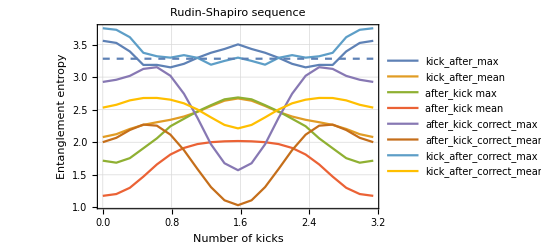

```mathematica
Show[ListLinePlot[{kawrsnmax,kawrsnmean,wrsnmax,wrsnmean,rdnmax,rdmean,kacrsnmax,kacrsnmean},PlotTheme->"Detailed",PlotLegends->{"kick_after_max","kick_after_mean","after_kick max","after_kick mean","after_kick_correct_max","after_kick_correct_mean","kick_after_correct_max","kick_after_correct_mean"}],Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],FrameLabel->{{HoldForm[Entanglement entropy],None},{HoldForm[Number of kicks],None}},PlotLabel->HoldForm["Rudin-Shapiro sequence"],LabelStyle->{FontFamily->"TeX Gyre Pagella",GrayLevel[0]},PlotRange->All]
```

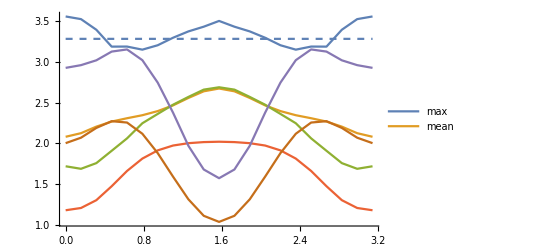

```mathematica
Show[Plot[0*x+c/.{c->3.281937853012085},{x,0,3.142},PlotStyle->Dashed],ListLinePlot[{kawrsnmax,kawrsnmean,wrsnmax,wrsnmean,rdnmax,rdmean},PlotLegends->{"max","mean"}],PlotRange->All]
```

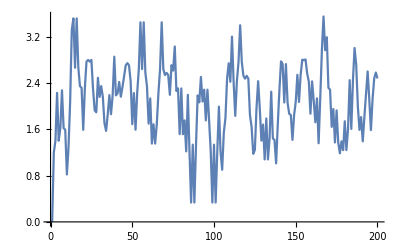

```mathematica
ListLinePlot[kawrsn[[1]]]
```